# Semi-Inclusive Deep Inelastic Scattering NNPSS Summer school, Yale, 2018 author: Alexei Prokudin email: prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/avp5627/GIT/WW-SIDIS

```mathematica
<<wwsidis.m
```

Package WW-SIDIS contains the set of TMDs calculated with WW approximation and SIDIS structure functions

Copyright: Alexei Prokudin (PSU Berks), Kemal Tezgin (UConn), Version 1.01 (06/05/2018)

e-mail: prokudin@jlab.org, kemal.tezgin@uconn.edu

https://github.com/prokudin/WW-SIDIS

If you use this package, please, site arXiv for this paper and https://github.com/prokudin/WW-SIDIS

___________________________________________________________________________

Contains the following functions:

f1u[x_,Q2_ ] is the unpolarised collinear PDF for u quark, bibitem{Martin:2009iq}

f1d[x_,Q2_ ] is the unpolarised collinear PDF for d quark, bibitem{Martin:2009iq}

f1ubar[x_,Q2_ ] is the unpolarised collinear PDF for ubar quark, bibitem{Martin:2009iq}

f1dbar[x_,Q2_ ] is the unpolarised collinear PDF for dbar quark, bibitem{Martin:2009iq}

f1s[x_,Q2_ ] is the unpolarised collinear PDF for s quark, bibitem{Martin:2009iq}

f1sbar[x_,Q2_ ] is the unpolarised collinear PDF for sbar quark, bibitem{Martin:2009iq}

D1u[pion_, z_, Q2_ ] is the unpolarised collinear FF for u quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1d[pion_, z_, Q2_ ] is the unpolarised collinear FF for dbar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1ubar[pion_, z_, Q2_ ] is the unpolarised collinear FF for ubar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1dbar[pion_, z_, Q2_ ] is the unpolarised collinear FF for dbar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1s[pion_, z_, Q2_ ] is the unpolarised collinear FF for s quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

D1sbar[pion_, z_, Q2_ ] is the unpolarised collinear FF for sbar quark, pion = pi+ or pi-, bibitem{deFlorian:2007aj}

g1u[x_,Q2_ ] is the helicity collinear PDF for u quark, bibitem{Gluck:1998xa}

g1d[x_,Q2_ ] is the helicity collinear PDF for d quark, bibitem{Gluck:1998xa}

g1ubar[x_,Q2_ ] is the helicity collinear PDF for ubar quark, bibitem{Gluck:1998xa}

g1dbar[x_,Q2_ ] is the helicity collinear PDF for dbar quark, bibitem{Gluck:1998xa}

g1s[x_,Q2_ ] is the helicity collinear PDF for s quark, bibitem{Gluck:1998xa}

g1sbar[x_,Q2_ ] is the helicity collinear PDF for sbar quark, bibitem{Gluck:1998xa}

H1perpFavFirstMoment[x_, Q2_] the first moment of Collins FF favoured, bibitem{Anselmino:2013vqa}

H1perpUnfFirstMoment[x_, Q2_] the first moment of Collins FF unfavoured, bibitem{Anselmino:2013vqa}

f1TperpuFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for u quark, bibitem{Anselmino:2011gs}

f1TperpdFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for d quark, bibitem{Anselmino:2011gs}

f1TperpubarFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for ubar quark, bibitem{Anselmino:2011gs}

f1TperpdbarFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for dbar quark, bibitem{Anselmino:2011gs}

f1TperpsFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for s quark, bibitem{Anselmino:2011gs}

f1TperpsbarFirstMoment[x_,Q2_] the first moment of f_(1  T)^⊥ Sivers PDF for sbar quark, bibitem{Anselmino:2011gs}

h1TperpuSecondMoment[x_,Q2_] the second moment of pretzelosity for u quark, bibitem{Lefky:2014eia};

h1TperpdSecondMoment[x_,Q2_] the second moment of pretzelosity for d quark, bibitem{Lefky:2014eia};

h1perpuFirstMoment[x_,Q2_] the first moment of Boer-Mulders function for u quark, bibitem{Barone:2009hw};

h1perpdFirstMoment[x_,Q2_] the first moment of Boer-Mulders function for d quark, bibitem{Barone:2009hw};

h1Lu[x_,Q2_ ] is the h_(1  L)^⊥ PDF for u quark, this work

h1Ld[x_,Q2_ ] is the h_(1  L)^⊥ PDF for u quark, this work

g1Tperpu[x_,Q2_ ] is the g_(1  T)^⊥ PDF for u quark, this work

g1Tperpd[x_,Q2_ ] is the g_(1  T)^⊥ PDF for d quark, this work

ALL[pion_, x_, z_, Q2_, PT_] is the A_LL asymmetry

AUTSivers[pion_, x_, z_, Q2_, PT_] is the Sivers A_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AUTCollins[pion_, x_, z_, Q2_, PT_] is the Collins A_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]]) asymmetry

AUTh1tp[pion_, x_, z_, Q2_, PT_] is the Pretzelosity A_UT^(TraditionalForm`sin[3\ SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AUUcos2phi[pion_, x_, z_, Q2_, PT_] is the Boer-Mulders A_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]]) asymmetry

ALT[pion_, x_, z_, Q2_, PT_] is the Double Spin A_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AULsin2phi[pion_, x_, z_, Q2_, PT_] is the Kotzinian-Mulders A_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]]) asymmetry

ALTcosPhi[pion_, x_, z_, Q2_, PT_] is the A_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]]) asymmetry

AULsinphi[pion_, x_, z_, Q2_, PT_] is the A_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]]) asymmetry

ALLcosphi[pion_, x_, z_, Q2_, PT_] is the A_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]]) asymmetry

ALTcos2PhiminusPhiS[pion_, x_, z_, Q2_, PT_] is the A_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

AUUcosphi[pion_, x_, z_, Q2_, PT_] is the A_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]]) asymmetry

AUTsinphiS[pion_, x_, z_, Q2_, PT_] is the A_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]]) asymmetry

AUTsin2PhiminusPhiS[pion_, x_, z_, Q2_, PT_] is the A_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]]) asymmetry

Semi-Inclusive Deep Inelastic Cross Section, CrossSection[pion_,x_,z_,Q2_,PT_,energy_,phih_,phiS_,helicity_,targetpolarization_] calculates the differential cross section of specified pion_,x_,z_,Q2_,PT_,energy_,phih_,phiS_,helicity_,targetpolarization_

Contains the following constants:

avp unpolarized D_1 TMD fragmentation distribution width

avk unpolarized f_1 TMD  width

avkg helicity g_1TMD width

avks f_(1  T)^⊥ (Sivers function) TMD width

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from Grids/mstw2008lo.00.dat

## Asymmetries SIDIS analytical calculation of all terms in SIDIS cross section using Bacchetta et al JHEP02 (2007) 093

## Definitions, Structure Functions, Convolutions, Etc :

```mathematica
Format[PhT]:=Subscript[P, hT];
Format[kt]:=Subscript[k, T];
Format[pt]:=Subscript[P, T];
Format[f1]:=Subscript[f, 1];
Format[hh1]:=Subscript[h, 1];
Format[hh1L]:=Subscript[h, 1L]^FIRST;
Format[g1]:=Subscript[g, 1];
Format[g1T]:=Subscript[g, 1T]^FIRST;
Format[H1FirstMoment] := Subscript[H, 1]^(perp FIRST);
Format[h1TperpSecondMoment] := Subscript[h, 1T]^(perp Second);
Format[f1TperpFirstMoment] := Subscript[f, 1T]^(perp FIRST);
Format[h1perpFirstMoment] := Subscript[h, 1]^(perp FIRST);
Format[D1]:=Subscript[D, 1];
Format[MBoerMulders]:=Subscript[M, BoerMulders];
Format[MCOLLINS]:=Subscript[M, COLLINS];
Format[MSIVERS]:=Subscript[M, SIVERS];
Format[Mhadron]:=Subscript[M, hadron];
Format[NBM]:=Subscript[N, BM];
Format[NCOLLINS]:= Subscript[N, COLLINS] ;
Format[NSIVERS]:=Subscript[N, SIVERS];
Format[kta]:=Subscript[k, TA]^2;
Format[pta]:=Subscript[p, TA]^2;
Format[ptC]:=Subscript[p, TCOLLINS]^2;
Format[ktg1]:=Subscript[k, Tg1]^2;
Format[kth1L]:=Subscript[k, Th1L]^2;
Format[ktg1T]:=Subscript[k, Tg1T]^2;
Format[kth1]:=Subscript[k, Th1]^2;
Format[kthL]:=Subscript[k, ThL]^2;
Format[ktBM]:=Subscript[k, TBM]^2;
Format[hh1]:=Subscript[hh, 1];
Format[ktS]:=Subscript[k, TSIVERS]^2;
Format[ktP]:=Subscript[k, TPRETZELOSITY]^2;
Format[ktBM]:=Subscript[k, BOERMULDERS]^2;
$Assumptions={z>0,Subscript[p, TA]^2>0,Subscript[k, TA]^2>0,Subscript[k, Tg1T]^2>0,Subscript[k, Th1L]^2>0,Subscript[k, Th1]^2>0,Subscript[k, BOERMULDERS]^2>0,Subscript[M, COLLINS]>0,ktH1>0,Subscript[M, BoerMulders]>0,Subscript[M, SIVERS]>0,z>0,z^2+Re[1/Subscript[k, Tg1T]^2] Subscript[p, TA]^2≥0&&((Re[Subscript[P, hT]]==0&&Im[Subscript[P, hT]]>0)||Re[Subscript[P, hT]]>0),Re[Subscript[P, hT]]>0||(Re[Subscript[P, hT]]≥0&&Im[Subscript[P, hT]]>0),z^2 Re[Subscript[k, Tg1T]^2]+Subscript[p, TA]^2>0,Re[1/MCollins^2] Subscript[p, TA]^2>-1,Re[Subscript[k, TSIVERS]^2]>0,Re[Subscript[k, TPRETZELOSITY]^2]>0,Re[Subscript[k, BOERMULDERS]^2]>0,Re[Subscript[p, TCOLLINS]^2]>0,PhT >0,ptC >0,Re[Subscript[P, hT]/Subscript[p, TCOLLINS]^2]≥0,Im[Subscript[P, hT]/Subscript[p, TCOLLINS]^2]>0,ptC+z^2 Re[kth1]>0, Re[kth1]>0,Re[ktP]>0,Re[ktBM]>0,Re[pta]>0,Re[pta+ktg1 z^2]>0,z^2 Re[ktg1]+Re[pta]>0,Re[pta+ktg1 z^2]>0,Re[kth1L]>0, Re[pta+kta z^2]>0,  Re[pta+ktS z^2]>0, Re[(PhT z)/pta]>0, Re[(PhT z)/pta]>0}
```

{z>0,p_TA^2>0,k_TA^2>0,k_Tg1T^2>0,k_Th1L^2>0,k_Th1^2>0,k_BOERMULDERS^2>0,M_COLLINS>0,ktH1>0,M_BoerMulders>0,M_SIVERS>0,z>0,z^2+Re[1/k_Tg1T^2] p_TA^2≥0&&((Re[P_hT]==0&&Im[P_hT]>0)||Re[P_hT]>0),Re[P_hT]>0||(Re[P_hT]≥0&&Im[P_hT]>0),z^2 Re[k_Tg1T^2]+p_TA^2>0,Re[1/MCollins^2] p_TA^2>-1,Re[k_TSIVERS^2]>0,Re[k_TPRETZELOSITY^2]>0,Re[k_BOERMULDERS^2]>0,Re[p_TCOLLINS^2]>0,P_hT>0,p_TCOLLINS^2>0,Re[P_hT/p_TCOLLINS^2]≥0,Im[P_hT/p_TCOLLINS^2]>0,p_TCOLLINS^2+z^2 Re[k_Th1^2]>0,Re[k_Th1^2]>0,Re[k_TPRETZELOSITY^2]>0,Re[k_BOERMULDERS^2]>0,Re[p_TA^2]>0,Re[p_TA^2+k_Tg1^2 z^2]>0,z^2 Re[k_Tg1^2]+Re[p_TA^2]>0,Re[p_TA^2+k_Tg1^2 z^2]>0,Re[k_Th1L^2]>0,Re[p_TA^2+k_TA^2 z^2]>0,Re[p_TA^2+k_TSIVERS^2 z^2]>0,Re[(P_hT z)/p_TA^2]>0,Re[(P_hT z)/p_TA^2]>0}

#### Moments :

k_T and p_Tmoments in Piet' s definition are

f_1^(n)(x) = ∫(k_T^2/(2 M^2))^n f_1(x,k_T)ⅆ^2 k_T=∫_0^∞ ∫_0^(2π) f_1(x,k_T)(k_T^2/(2 M^2))^n k_T ⅆ k_Tⅆφ
D_1^(n)(z) = ∫(p_T^2/(2 M_h^2))^n D_1(z,-zp_T)ⅆ^2 p_T=∫_0^∞ ∫_0^(2π) D_1(z,-zp_T)(p_T^2/(2 M^2))^n p_T ⅆ p_Tⅆφ

I will include -zk_Tinto the definition of Fragmentation functions

```mathematica
XMomentTMD[n_,func_]:=∫_0^∞ ∫_0^(2 π) kt (kt^2/(2 M^2))^n func[kt^2]ⅆphiⅆkt
ZMomentTMD[n_,func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt^2/(2 z^2 Mhadron^2))^n func[pt^2]ⅆphiⅆpt
ZHalfMomentTMD[func_]:= ∫_0^∞ ∫_0^(2 π) pt (pt/(2 z Mhadron)) func[pt^2]ⅆphiⅆpt
```

#### Convolution is defined as Eq. 2.17 (compare to formula 4.1 of Bacchetta et al) C[wfD] = x ∑_a e_a^2∫ⅆ^2 p_Tⅆ^2 k_T δ^(2)(p_T-k_T-P_hT/z)w(p_T,k_T)f^a(x,p_T^2)D^a(z,z^2k_T^2) fragmentation functions are defined with respect to vector P_T=-zk_T , we will also use the following: k_T=p_T so that, for example D^a(z) = ∫ⅆ^2 P_TD^a(z,P_T^2) =z^2∫ⅆ^2 k_TD^a(z,z^2k_T^2) . Convolution can be rewritten as C[wfD] = x ∑_a e_a^2∫ⅆ^2 k_Tⅆ^2 P_T δ^(2)(z k_T+P_T-P_hT)w(k_T,-KP_T/z)f^a(x,k_T^2)D^a(z, P_T^2) which we will use in the following

```mathematica
(*Eq. 2.17*)
ConvolutionTMD[weight_,f_,D_]:=∫_0^∞ ∫_0^(2 π) kt weight[kt,PhT,phi] f[kt^2]D[z z kt kt+ PhT PhT - 2 kt PhT z Cos[phi]]ⅆphiⅆkt
PTConvolutionTMD[PTweight_,weight_,f_,D_]:= ∫_0^∞ ∫_0^(2 π) PhT PTweight[PhT] ConvolutionTMD[weight,f,D] ⅆphiⅆPhT
```

#### Distributions and fragmentation function:

```mathematica
f1[kt2_] := f1 1/(π kta) Exp[-kt2/kta]; (* unpolarised distribution A.1 *)
D1[pt2_] := D1 1/(π pta) Exp[-pt2/pta]; (* unpolarised fragmentation A.1*)
g1[kt2_] := g1 1/(π ktg1) Exp[-kt2/ktg1]; (* helicity distribution A.2*)
h1[kt2_] :=  hh1 1/(π kth1) Exp[-kt2/kth1]; (* transversity distribution Torino notations A.6*)
g1T[kt2_] := g1T (2 M^2)/(π ktg1T^2)Exp[-kt2/ktg1T];
(* g1T distribution Amsterdam notations B.9.a*)
gT[kt2_] := gT 1/(π ktg1T)Exp[-kt2/ktg1T];
(* gT distribution, using directly WW relation of gT(x) and Gauss model B.9.c*)
h1Lperp[kt2_] := hh1L (2 M^2)/(π kth1L^2)Exp[-kt2/kth1L];
(* h1L distribution (Kotzinian-Mulders) Amsterdam notations B.9.b*)
hL[kt2_] := hL 1/(π kthL)Exp[-kt2/kthL];
(* twist-3 function hL distribution Amsterdam notations using directly WW relation of hL(x) and Gauss model B.9.f*)
gTperp[kt2_] := gTperpSecondMoment (2 M^4)/(π ktgT^3) Exp[-kt2/ktgT];
(* twist-3 function gTperp distribution Amsterdam notations using directly WW relation of hL(x) and Gauss model B.9.d*)
fT[kt2_] := fT 1/(π ktfT)Exp[-kt2/ktfT];
(* fT distribution PETER VERSION, using directly WW relation of fT(x) and Gauss model ZERO UNDER SUM RULE B.4*)
hTperp[kt2_] := hTperpFirstMoment (2 M^2)/(π kth1^2)Exp[-kt2/kth1];
(* h1Tperp distribution Amsterdam notations, assuming the same width as h1 B.9.g*)
hT[kt2_] := hTFirstMoment (2 M^2)/(π kth1^2)Exp[-kt2/kth1];
(* h1Tperp distribution Amsterdam notations, assuming the same width as h1 B.9.h*)
h[kt2_] := h 1/(π kth)Exp[-kt2/kth];
(* h twist-3 distribution ZERO UNDER SUM RULE B.4*)
fperp[kt2_] := fperpFirstMoment (2 M^2)/(π ktf^2)Exp[-kt2/ktf];
(* fperp distribution Amsterdam notations B.9.j*)
fTperp[kt2_] := fTperpSecondMoment (2 M^4)/(π ktfT^3)Exp[-kt2/ktfT];
(* fTperp twist-3 distribution Amsterdam notations B.9.i*)
H1perp[pt2_] := H1FirstMoment (2 z^2 Mhadron^2)/(π ptC^2) Exp[-pt2/ptC] ; 
(* Collins function A.14*)
f1Tperp[pt2_]:=f1TperpFirstMoment (2 M^2)/(π ktS^2) Exp[-pt2/ktS];
(*Sivers function A.5*)
h1Tperp[kt2_] :=   h1TperpSecondMoment  (2 M^4)/(π ktP^3) Exp[-kt2/ktP];
(* h1Tperp pretzelosity distribution Amsterdam notations A.25*)
h1perp[kt2_] :=   h1perpFirstMoment  (2 M^2)/(π ktBM^2) Exp[-kt2/ktBM];
(* h1perp distribution Boer-Mulders Amsterdam notations A.19*)
```

#### Moments of distributions and fragmentation function:

k_TA^2 = 0.25 (GeV^2), p_TA^2 = 0.2 (GeV^2)for us 

Integrating over kt only :

definitions are such that

f_1(x) = ∫f_1(x,p_T)ⅆ^2 p_T=∫_0^∞ ∫_0^(2π) f_1(x,p_T)p_T ⅆ p_Tⅆφ
D_1(z) = z^2∫D_1(z,-zk_T)ⅆ^2 k_T=z^2∫_0^∞ ∫_0^(2π) D_1(z,-zk_T)k_T ⅆ k_Tⅆφ

I already included -zk_T in the definition on D_1 see above.

```mathematica
Print["f_1(x) = "]
XMomentTMD[0,f1]
Print["f_1^(1)(x) = "]
XMomentTMD[1,f1]
```

f_1(x) =

ConditionalExpression[f_1,Re[k_TA^2]>0]

f_1^(1)(x) =

ConditionalExpression[(f_1 k_TA^2)/(2 M^2),Re[k_TA^2]>0]

```mathematica
Print["D_1(z) = "]
ZMomentTMD[0,D1]
Print["D_1^(1)(z) = "]
ZMomentTMD[1,D1]
```

D_1(z) =

D_1

D_1^(1)(z) =

(D_1 p_TA^2)/(2 M_hadron^2 z^2)

Integrating over kt only :

```mathematica
Print["h_1^(0)(x) = "]
XMomentTMD[0,h1]
Print["h_1^(1)(x) = "]
XMomentTMD[1,h1]
```

h_1^(0)(x) =

hh_1

h_1^(1)(x) =

(hh_1 k_Th1^2)/(2 M^2)

```mathematica
Print["h_(1  L)^(⊥(0))(x) = "]
XMomentTMD[0,h1Lperp]
Print["h_(1  L)^(⊥(1))(x) = "]
XMomentTMD[1,h1Lperp]
```

h_(1  L)^(⊥(0))(x) =

(2 h_L^FIRST M^2)/k_Th1L^2

h_(1  L)^(⊥(1))(x) =

h_L^FIRST

```mathematica
Print["h_1^(⊥(0))(x) = "]
XMomentTMD[0,h1perp]
Print["h_1^(⊥(1))(x) = "]
XMomentTMD[1,h1perp]
```

h_1^(⊥(0))(x) =

(2 h_1^(FIRST perp) M^2)/k_BOERMULDERS^2

h_1^(⊥(1))(x) =

h_1^(FIRST perp)

```mathematica
Print["h_(1  T)^(⊥(1))(x) = "]
XMomentTMD[2,h1Tperp]
```

h_(1  T)^(⊥(1))(x) =

h_T^(perp Second)

```mathematica
Print["H_1^(⊥(1))(z) = "]
ZMomentTMD[1,H1perp]
```

H_1^(⊥(1))(z) =

H_1^(FIRST perp)

```mathematica
Print["f_(1  T)^(⊥(0))(x) = "]
XMomentTMD[0,f1Tperp]
Print["f_(1  T)^(⊥(1))(x) = "]
 XMomentTMD[1,f1Tperp]
```

f_(1  T)^(⊥(0))(x) =

ConditionalExpression[(2 f_T^(FIRST perp) M^2)/k_TSIVERS^2,Re[k_TSIVERS^2]>0]

f_(1  T)^(⊥(1))(x) =

ConditionalExpression[f_T^(FIRST perp),Re[k_TSIVERS^2]>0]

## Omegas from Eq.(2.20):

```mathematica
(* *)
Clear[z,M,Mhadron];
omega0[kt_,PhT_,phi_] := 1;
omega1A[kt_,PhT_,phi_] := (PhT - z kt Cos[phi])/(z Mhadron);
omega1B[kt_,PhT_,phi_] := (kt Cos[phi])/M;
omega2A[kt_,PhT_,phi_] := 1/(z M Mhadron)(2 kt Cos[phi] (PhT - z kt Cos[phi]));
omega2B[kt_,PhT_,phi_] := 1/(z M Mhadron)(-kt PhT Cos[phi] + z kt kt);
omega2AB[kt_,PhT_,phi_] := omega2A[kt,PhT,phi]+omega2B[kt,PhT,phi];
omega2C[kt_,PhT_,phi_] := (2(kt Cos[phi])^2-kt^2)/(2 M^2);
omega3[kt_,PhT_,phi_] := -1/(2z M^2 Mhadron)(2 kt Cos[phi] (kt PhT Cos[phi] - z kt kt) + kt^2(PhT - z kt Cos[phi]) - 4 (kt Cos[phi])^2 (PhT - z kt Cos[phi]));
```

## Leading Structure Functions and Asymmetries

Phenomenology of unpolarized structure function F_UU

## F_UU analytical result:

```mathematica
Clear[x,z,Q2];
Print["Eq(2.18 a) (*Cell[GraphicsData["PDF", "\<\
9E14ARda;S<:9LCUl^G[Yo>Pd<C62S@P<21_HVX:?3`P;daUKVMdJ20e830PDR0_
AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06MWD^c;CMeanOkDfb81o]F
:S_mOP`Hf0A`YIbZ^7aL6N0<S;4319_H@>b4hS_bKC;=KdUJJZUkMJ]kU`LnmmjS
U[@NooFDm>gmho^gmh[on[Uo=^=`Wk[j>Lggkkjlom_mVo/7KoNjN/kEG;]OdYnW
m]Vfdgg/Q^OHS_Ng[noon?HomJfn_geeonGmlOe_g]goXGYfmlNGgkfkEln67mkM
oognm/ogWkg]OK>^^fOG3o[AVomXNgLOOOcXgOg]MdNSVoiI]G6d;/V=_[6TgnZ:
o/P?KEdofo_SLoMS8l_ko]fmVEQUo;GoL;o?_k2EIW`>mlNO`/3Ym_SZcniOfMlg
n/<Go;?KJ?c27o@;lS/b8knn42Klf^gaQImI:=KFSOaBo48b<2kWbcQS9:e/PjU_
Sml_4ogJoId`h;ohZITL;n;@n:l9<I;UgPZLJ__a>CNmLR[@^P^Ln/n4DocNF7WA
2Cnf@oO/jiZagG<N0Y<7PlWE/jZZi_kfQBV0kLS`^DfFL1<93=oio1]fR;QD<WaO
hUY4OQ[F<]=i<Gkljn4n^ZYmSWdGmQ58/=k7KDMm>_AXJ^MTmDioo>XAeRLljmYN
V?HFE>TV6R@BLWm<kXMJa5Hhk_D/2<7m4GVKRI7kYB14]lOOg3368kC81Sml7gmK
A:8BkN3O4SWXhBCXh932ocPdcjV;610h>@H>==fHT4mQ@dK[c`XQ;G3C]Q]mCIOQ
m4Z19:YNe;Sh=oX[SU9]OALm_GWjA=6?Xn:64l4?a7AJ`KX2A8CYKnko>Hk]DbGK
eT8EN?Of^m^nB=KMm4@/kl<llolYT:D9E?ei@]?ZFEO3M4?0]dYFmlP>BSK<hg>/
i_2E:GcUddoMI`[:DHo]/hX;2NbM`bMnTRa46IXb]ikjImn/MU73O0c4kO7Cd^Ri
OZ8Lf8=A:H3LWk<3CEDmQfWBZ@n/b9I/CCDnYo4nX]Zc@8ncJWfHn2o_K]406D>1
k[X23[:a]EZ_:]Va=GS`i]@?3V_FROnJS;EXgC@Xh[;SC6@`ELUXHfKAoVKfPS90
HFo8MMWe<_QVC]dfP?RJclZZOeY66c;Jh6L8PS/I7NZ`jDRaI>X86JV4=Md<oX;M
QYCL7Sm>YPH0SRa9=dk?DBR@:U``9;nl?Cik=8;6P4TmOOkI^h299MgYVA=@6hKi
f@14WZa=<2bi5[>f@LcDUSTeI[H2HHMQO?JMbZ?Gh]_SXhoL7T/[2EZL;BCChR<`
2UZL3@iJO3nYaL?D?HNjEOJZK9CL^JS6fMaN;VnI<kRUFe3SPJf?KKmAhlF?=8H6
=@iSMMFZ3nODf9[hmSR]a]V>UEjHKTFOVk5/e;RJdD>AU;TkD6=KUe3SZNUDG<>^
MNZb6ToXXCWekG56SHLJ6OMRXR_G^A<m5T=Nd^=JH32SWb[b?E?TGn4FX=6WeKTN
@4WXdlk?JU3bjQYoWQP6]dCdgECW1W^6acSPnDjeORD2gQmonleW3oNYA:Fg[:iK
O?U^laEe_Q>m^VfMTkY[Wn0MBn3oEKB]JVU`=EG8;3PBehAeQoF_MN?_S`Ogn>]4
0Z_=nfGW2Vd/^inO<i[/USe6b^Vb?eUV=WBS7RB^1H]]/X/<a4ekWfZ?OBeHSZ70
;alDcj9;mNJnTW3><YOZDVER=0N[L=JUbPKWH7`4iLjU6^12ef5^_9UG2Dj4a/H7
mJWlg87c2X[Yj:fl:QQWe5O>WO>YMSRG@X/a;cX[:HYLFWGR58b=/OR1CTdLZiEJ
^]og4gfg^1cm/HaCB^]S7L<GNmI8n=2bPVILjeRjIG?ZESaG`=RHn_Kh<95dHm=P
`X@;:4[F3hX=jhQFTSOFF?a0]fb8?UaOM/nb2BjghWTSWi@iLmJ^^e5L=jaO]^/D
nEeZi_IX=>`ESli5a12D7d9<kGkh8QZ5Pb1=kD4eTB[CkBZ7=niMbAkP`@iMC::e
0@nl?A1/BU1UBoYX3o:_W0AF]@Lef=JYWeZ[URBbJP6[fX=/IQFHa78K0U>[>O1S
ELh=:gHo<0N/^ZdRhObZKho475PcZcW8EQf]L6X>2?PUa2jHPhY@Nm3laJhm<<<W
]@MNS0;>I<ki@O9:@na<1W=kL3CJf`=LTXKP9k<7^CFf5:hV[C3dH6^fl5YIWaP4
Lm]R4VI1VVbh`V/bfV1ODoO?VUQXb0A71OH_a`QGPa?SZ6=eegkRg5GMjUWC]<@a
;3ZC6ifhH4lH<oJbHBL[:^fjh`nBEE_TKUX4LD<_3cO50;lMWX=0:k[BhGmiCQ^L
/VR=nN_9P``Ek^mjdJTY<ZP558mThmg@<:WZaU_9OU9DJ06SG3`DG@_A28V_EY`m
A:cAk79DkWC=9Z47DQ8=XcMZ/K53Ih>AC<BmBI9ZA9YET8C]YF04OgIZkkgT;M@?
ENY/K8m;X6oiDb?=4gCY2K_8<0CmEm?caAonB2Qbd_CdZhmL/C`cHlTbKUgj<iIW
=K7:m3W3hcN^@Wg=k/RJUoS]V]UI4CcT5UMFib0UA:j_8BgLS`P1JF;?>=F/SmIA
R0Vo`NYhn@UO^6Qd<]VkJ7?8Cca[P?BbcIWabHLPmV6d8VQR<`a7Y@6oa5aU]5OT
;YT<2SFhU[Vhj;@YWVaec9VZQQFW>ZKCoSD1@F>X82j5ZIc=4LN:1Z>Y7NQWK5:8
B3995^ICjfc6f^UUdfZX[K[eXn=E=`>9J1Hm^>BWPTZ@l@:aZ9M@0=K1@C5E/;eL
kc_T3N7BB1HYTfTeT0F;8BE/X6@TedXfnV3AY/GX:N/:63^QSTIBJIeRTCEL8iM/
gJVE23GU<h7;UfL25n;3FYJ;jmh?^UaMkFWS@NIn5>=1f4JiA4WVhaJ<6nI3C1ZN
UTAL[XIh7<;ddi<Z`?8mElXmRLV397VAeikBNDc=9A7<D[@im>HkoUE`]L>mY170
kdW5caO<K/TV;6HZ[W[JQTmL1MJ<<ENA5E[<Y0H3@eCn4g0lc>h4X@S35N>BdBJd
^XYICcSG8Q5nI/Fh4[CjRUTHZjIHidEbHU[>0<R@gK4VcU?];R>k4l=9829iWYc[
4FKOol31GH7]?]f39i?aGGGZf97AM8mXDSFX:ReXNdR2T2ZBaM?4/:IO2[NF]3KT
TB]De5Yf>EG4F:Md;bbk6g6N0=`GU`eFe6@`nhf/GgKA9eAND2cSF`ZnBn7_:o1/
94/D8KHP4gF;Sd?1X:mM=Co`AVERPk=k2J:^`FoQ:cS[e9EE[h>G3]2B8WX=J><7
Gd5Jih:Z[;j0]1Qjd^Pm<K4T0EI8jhZJIi7FDcMlhR[BIZbiR[CHdA7UNAEY/hD[
hYe3FT9CDInGT=J?GB?5BJ@e9Wh1JC>^_hZd6OUDZdhR;M:[nJj;>4_VJIQY^=U]
TK3LJ@A52Vfm7ia9>bGla<KI63doQ`6/=3OlhC;J//cdAm2IdEoO;gPhh_V79Ao]
ee`c]CZY^_LK5KT<d2@hl>SbcM_h;8e]10oWlIU^c7VnMi=d_bQ;EI1>`g=CBHmC
=d_a@Ue6>Qg0=8XF;WgOWTnR[3ic;H_BcLfcad05fE@7k5PUG:/In9g?[4ZAQRiK
od_cmf6/2/U9WcfDLfGEe6cbEIo;ggN[EDLTFFEBjTXhHeKSB@IGm;MeA>MSK9V8
7_nEC4X@Xk2?RgHXUl6[MXR6/FQ3@h]L>Gf__CGi^RnI8F7Mf:[0ZKbMLoS3F9DI
WMO[RXoa]`;G18OOVSPg@bHXPH8CCNgiSUGQSmE4OOAlIUFCa6QKl1mlm4hJZM[3
7SMSbl5fQ<4[fe5<RA3AEZR5_NFbkIP9AekJ<WJWVV[V;FkIi=C0/RO/URWI:BSI
XgeQb]hdEEl=:Llf4nDOl/I73SRTnO_OG6/VLWg?R28QWiSI0=TnBDJohO_^^06Y
TcmQde[Y8/JFl:=[bHjMc[mbOh?5ffl0_nGW2=86l;/dP9?Hm?gO9?cfn[mI0;mf
LjLSF5;/ZdISO?glLkMJ?_COkPLn57n7mK^2N_aMoblLDhSKdEoi;_aZg5i/dXio
XklB?omjJgNiZCeb9f3Dd[hm;b9TiU9ZH6XFZe;CR1O;6P2=LghfW/E^MHHj8CiD
if1;HjAPhcPa8_Ve<gd1U8SGglP/M>PG<R[/m0Dd=F@PTMbA7Mgg:n2af=RM=WCR
C9;W7Dio[9M42g^^2IfdGTlGCj1Wh<MY4c^@ARM`kXQMIP9Y_`dofWF3:1cH_1c9
XU<fb4N[dOPGU@@DZae^gg>::QbA^]MaFYBFV^/GGk]S4eoO4HZV6OW3knnOL>iZ
ig18?N9GdTX^QdBZ>FaIYoeHYmdK?0f^?C0G`>1FW>VlmifPWCAfmi7a>W]RkLcB
TRCD98nEcjhF?QU]fDZTY:4FfB4dKM>5OIme;FR:9:lMaZZlnXW;UGelVIY5nhW3
H9fhE=TW1Mk;QQ7aEYTE_E70o534T0JhQIi]b>g`h^nBhBj?2D?/he2=71JRTB<W
_6NKe9]o41B^hH`dPIDclXd4LL@C0T3>PgHaka12V`8ObM1=dn18<Rdi4QD2cD_^
7HeZY7eGo8L<@EGSdbICd`6@Y5hT`dYg/26A6hJkQL=Bhd<;:lMhlTKQ2R<OaiXC
B`68HUnnK=DKlXMa]34cA`ljYcDPLJ_]I568U69kN44;56Uo:8H`SK6`ZRSgOlWD
e/9KNU;T`96=LTW]c<Pad0f<3l?@jCU3>@n_6lmh0LIU;PN<]`DH0BgHEP36U_E?
56Ll<8KYPX`oo[NdCk@K;=iZVX_Fge]6Vl3FRRm>9RIW[mGaI9ZBU^iGCRcZl22G
ZQ;7n]ABH^b1HQ^NSS]XFmYQ11DbI3<5Jb^E[GSRi;33h1DN7l>R[;TVMa=PLHg7
7bcD]/W56E4ifk?3[0@FJM6SFF8G5]/AJ7MH]7;77==ol6XIL_T2B0HEG1S3DW8T
33G]U7>VLTV6XhUP]/:SA;V<VNWF`_e0^dPMPPY[6YI@PJcSLn;XGbja1XjJlXhf
^X9j?U[Qk1Q81DT2kl7A/>L5AaLT]2SFXFR3B7/6oj[TF;437>eX>R>CDfKEU/dj
5433IXDeVhYR;QYa[nQ=N@f1>a:^SMSJe4UEDV>^oHhG58fo_`9A=PoQ2QSJLC8=
[akjRW=iP:5>/EaQb]ja]5;^:NQk?ehGCTndbffl5hff/c=hloTcN4S@A:FTAH>W
f?VhN`K?KGD[6=Qd=S[LFoYUjdR`81V4/U:1Pd59?M3h1ZGFN^[FgkPBRTe/0heL
RX3ZWZHJhEQ68MQ<Mb9M064k=M:P7oR^B_WAQEQ/E8869E54nHT:jUiP4X:RUWAi
SGogBRc6g=UXEI8HRgf;QnX>RLHH[2G5gg?0MG4e;/EP;CF8]UH@doW>1V6ij5d?
`[00dZdCXVnM?C4j9WI[49K?O/kIJ0102L94g?]N4iHZK:Gl[Po2`UQMm[DP;1n/
4amk6`fmcA:41N5NXoOk1LV<@MR6g4H@APbejfeX49HCg[?=1F4T[fSd?AN1hGga
7APQ::lW][a_WFOh]gPSdE]71==:WbZ9Q20o:P69if3;3a7HA2]L_PgElc<Af0A>
QM616BZkaii30eB?^9bbl8[kAOc25JG>Q60SiJAlgC[cL@SFL/:=<Ve;<HScPV/9
BRQVnj_hF]979?N9c;6PMCh2XenBHb`f]_eRTMjM2:agHR9M=H5PQa5HV<_3HQ:1
DMbVG5c`7^@FVhYO2k0HiP/BOR84`c6D;<e6dDk6H0CX>1diOlo:ID^OIlDYZe`^
EBLBC3ELlIIL?GERALF`K@FWDPQ6RXOc@CV`VJkUEY=K3RA8Ij@=alNXf98jWAbi
DY<O?IMb34I<S^7LHMJE64b^MMYCbaml>g8Q1R>=BoG>`/9kMQN0iJZ:FTW/WC=N
HJ4DPm5EBWPIL24`?]:`Q0]M=D^K[DhMQQ/BJn9`Agm1Ab]f;^njl6<TkKP=Rhdc
eR5Y0;@5BIL`bR9IAo]J9hRD^lh^j;g9QEQ7@AQeah6TOiUIFg7_M:`gG5MQF4YZ
dXGj6Pa;I3AbcIT=`coCCBl^IQb`MS5YFj62FH3B3_DT?J=@^[:CJCJ[48WQ:0`L
DUcde?GdZIP@RZgRTa>QV5bST:^;aV9IiG>F:^BUTd/Q8Z=K^6XdFJh[gAC7BQ4I
GTk;4C?eKYJnVoF>]h8VQfIMA9IoHhW8UVC_GW4<2/T]J?5bUj@ALU6?hn:HSlP@
>jkN2m]@3Ogdg>D^[SZ6WVH4EG`i7I5QI42Z39g>E/NH>a^]c3b:b7XiL36l795Q
ao]>fiee_]<AVJND2/gi2jUlFJc5=IIk]Ej=b;;IcoTN<B9c9AUEV/GgF8A]:nH=
OH=B5V_mF5gfaHP/6j`C7o/N<B;c`[d6l[<AfIKLATAfU?n=4EU6N2ld=eLD:nE^
G30/D:g>]FYXd[]YF^n6:A/9BXfYG@ahH4<Kl]l=H]IBBZ>?<Y1_hmJK2N^6a_RF
f4UBl6g/d3[]/W3fbmemURmK8BD9o^a=TejJg<8M`PN1DbDmMUVJRO8EMfK9`Y]N
=jgTCYd>bfEYIU15g7^3g;O7lITgJ_BTCQT:VjlO0I>ZE4/=Ebjf93/@V:DD:iOO
i00=a/B0dM/S2Oj//8AVTdiL2:hdJ?M_k5Pbae8YM9=i2;hNoM4D81cb49aamgHZ
nY<ShE^U?Qom@NF<_d[UA2k]05f2?aYn`nS0Xg<0k88o4YHiR2X>UX<onZQGHh<b
LZ>L>YFV9X]8S29H9_8O0k0;oVAXjUc4NOfiY_gSU2fifPhGMXMEBNa7nhoP[nBL
;JfDFeYk:/<iea@?l_ZKOK=<2bXd4T:m08D]_C2E^;8I52ZRO5BXj;MDm=/MA;To
BW6Sa9a2O`LYJo^Gl]dRVmC^Y2<U9i]DVigmBi<EiW2:M`>m2?U`YKZR/5g_U2XD
9j8LcD3QX>=:/a8:BoG>1KaNBl>nMNIdm=IITA;Li>S]S5jHNC5jRd]n==H`NRDm
hcHeeg8Ja2@/F[NLf7UCa3^f:TU7SoiQeAjGKXlBnWM8IXm[HJ5ohRBT<FLH/7JR
CaKoY>LD>39mj2/a9fE]:FQ5MkP@LiYB6Vi]bZEd^D=LKZ1`3JB=JcJU]GAkJa?]
V8Bco=?IFi]Vd^4]YG`l/iE`K/;?@VmVBkM=_a`heV<O5gXcIBGI=bj6We@VJmXC
@bbR1RUE/^>28;fIm=a@gJ:YIZgX9blGeOPcXjPJiM?a9dgbg7NfDQfh7SeTBgaZ
eid9AVJS5FZ>hTnY/b>l[eH4YNMYe?I4WNmdo>TYYDbk77mbcd5bHTIWC`b2jIIc
/_gIRcg?Ien`mISD/J2H/OVLmaC3EkVQ==kEYL9jk3g5l3DK6kfHe8Y^CH8LbgHf
e0l>fZhC7g]?<Gc=M2?6D:O3Ei]KRO]DJ5n:hF_6=nGj3i@CUo3E=^L=B2nWVeXi
ZaI3Q;>f3@N0:l1aOC?6jo`O9QYZd9lhE6hfKX6Y<IiAFTC^b9cSl=6::MPTnG=E
5QFhU>lF<S@dOG6jN;GZdkejg:e4hH<Xab3jkJ7NTnf]=ZB2FnTiHN5MK79@LZO@
K2jLJmE`mWGVUH4ZaK1/F/Y<<5XjcS@[6W;f9IZi`YhDRfQ4UVi@?ebA?75SC7aY
YOhYZG<CRhmMiEKJM2AO8JkSoX<@JA2[TjeaO=e4JZnEIX5IJ/`Nal=>EJIC7lQR
TDPcM`:bFPO4PDGQi=gmlEjR4^I`KV=3X7?A2Y:IEoG=dEbMd0eA?/;BEBeB8k1E
Ao6b1ZO:=Ph_5/0J:agM/2R3dY<hg883CYLc4?LhW1oL/bHV3`Ji;1Rn?lXEC2B;
0kXk_4YP>4BaNlge;IM]CIWi57MGABJ_H=Zh857/:76`0HHig`dR<9HlGXJ5RRRU
h4ARf76>0[M2U6?5U0M>Y=_jADBA1T=a/g9IEdA94SJVU/[1XlWI;NN[[kCd68@k
R3a9d/F3L=RdTZ`4`_;/RZC<COA?1flieG5OAbdC6ec>jm@7Hig9DeaAgDkQfaX[
5bJ^c:G^]iCVh<DUWbl^8Om>m8^@L4ET@?jEP2e5Dlb@kl^C6ZdO/4;_MM7D5P^i
gY5kdL[PGBZJdVD/nITM67niJ9XiBWKAm=OGRjI]emhK6/4hDk^Rl2IZgBfJ8]DL
eN3>@011SfZTUaFT_Z@=H_CN^<;fjQ]WXeIaa`LF8=dP6Vk6X^TWRN4/5De91O9X
4@O=<6ONCe5Iom@ORTjJLBdcFXNX=JNX8]?IZ;G1FI/h4I9jB^N[Y_UX=BD7DF]3
5d^31GTaJQFWU]NdE];cLD9eTe;Q<66PE=S[iCiF>OHcaJKSj2bU3X/e^hJMnN`:
RLUXXcBRHJN8fcbmESD=HgGGO^;KXo0620PPHFLnf0XkcBgS@3M@:U1<cH3:agVG
ABi4U7]25mYU;X]_QTcdI6]D:7aja22T4ALReKCK`b_JOPFQT@NX:6/]ll/3IkZ?
a?4`NQZUnXUZBb`Ukh_iRDe_db@Q9HN1mHJIUHA;h;Uh^^I`FYjhYUV7QmWm`X_A
7a3MLkkGEC9S@hF2DnXkF3=;2jXl3i8_G4VFS]hbB`Yk5EUXTfKinEMcJV:`PA>4
/XB1XbPYY]gC9;IYU9da9Sb`<Ne3aIPTPY?@b`e`V;JD8DlU/E/iH/mAQP1Y:`jE
0cQYdLE7/c4Y2N3<_MHLeJa83SBBOeM2WDl]B5f7gVRAL6Xl@CK?8YX48E2Idn5;
fUN1YI188bTP<EPn=ZYDVV[MbQH?gi2E@2kma67A>W4YT@H<h<Hg=:W9na2I;]nF
26jASDI9A=6cXaXDkAeKX;noe5DWelC8<FMi7@`<38]Efii^e=83^FQMcQi;1ZV>
3l05PgEkG85O>CKBi6:RZ/aIK4Un7J<_QM^9Z4m`E6iJC=6G=b5EYcih<jFDjXIL
BV1?7aGB;3YSODP0@@::cg0n4=12Cd=B:1_gPYf^nQMm?3FLJA1SDYmkPi7AE;>D
LDVhJ8HQP[Qbf=4?3X]FNQm7RhfkbHP=4iP/UjL^X;gT:LdeP`Nc@7jjJYfhU;6C
9a9OXkBP5nY[4U[:WL^R]eaZJDZVF[TJ[1]>A<^TM2/gP^2oLc^eW;UI:ERB:;A7
TlVIdF81@1EZYMH_SUO]BVD<97e5R]C[`dH/5abAW96KbN?8HV?T8[hC1ad0_HYl
J<2AZdJ6mU:fV4^5IBD:nGn2NUh3FUTKYIMLjK30R9gnUk[b@4]Cd>Hm/YU84<Mj
K@jL?RdW<6XD1g2[6:GKINE`RM`]m]:R^LIkhW[HX1UQdM7BUB18CP_:>cSIZSd8
gAhU46[10P;JK:`bjaR3^PYY`id86;@RMN[jFAQ4@b[B]T=ZknW_gJXVYja7/Uf_
T;[3e0h>LjGGCo_eC59_@DS>=TbBeLQ<QAN^LW@QKBHEakD220FaEV>AP91Y7C^/
O4M5bP:Q938aXTYYDI5H::1@h=<12/FYe]j<M>iU5ek/[1BOSfZ<QD;g[>6^T>hR
UY>kWX=OXeZQ`[Tm8f2:FNSGb>CkaGJ=DgOE2he``/CoW3^e=;[VCN9[]ef3d@8V
h][A:jTNJ3P]L;9M8bBnlVmLC7aAoiR1Qk00mIoca9Llo;5gOY^ZY>@E/;lmBYHk
Q9^7?dc[6a=O6DEEKDhW_RAAS<_SEj3PF7:]]EfSbDH[=hlBGaQn>G<K0`4Pjl8U
FPfoc[/0@NAe_]>9;dlYIM[EMXf6ldaTaWFhcYjT[TbeegJ=8?TjO8<cV6e;DF?N
;6?cfBSCWonFBbliXABVEV4]A9VhG7;J81lK3L;9_9VO>?1;9djSC7?;8FmV4_aJ
h1KbIQWSUG6Dn/ZAVk/n6A_1WC/La0hD==`VToDBkm4?V7=NYclfCV;>^>o6CD`i
Gd5NnEibOJCaGbi:b:MFmBki?Pf=oaggm>FSMN69mf?UnjC02JFTH`NHF56/i?e8
hklLk``c[a@m7Kge@]Y:;]RGVNGPX<hL9?I<fXck6O0SZ1QFI6IB@3bA=B?AdO=j
RPf8A^E<VRcL00n8BdBc[YbIX22W56[9ZWXl38_e33[A^bnZ;@6=3FQW/fJeG:92
n9MCZRQK8BDT/3R=:]PZe`VH6QjK_<7T/VIhf4]KS<9:0LldJiJ=SGRFF[b]J8Th
^ZbI7gb0IlIH5ReI/iYRGALK8j=Ha[j79M[E[5U=UHSTCKBEei9Vg3E2]:S54_D;
dWfJf:]9<mj/BQYREKB^9leb:E4<XM_]1?Kja_NJ^g:4P;VCU:@fM[2GHnKTf^ci
?eabKYJLT@jAfeJ5IL>TcZYU/@efbh^T74kQe:eDN<>Z8k_;`<fDCUYBiC:c3BKk
Z?4=i:C]GBO8KNeJKXVQMl^]G3aGMdfTf[XDNlfIdNNA19PeLoW85^XUNoCd3S@k
AnnFaQKY00_d?S:DFfH92T_j?FOFfL1ENVUJ:Am`hXbP9<O1D]`ZWG;bj8Qc3dUQ
nM6Z7lO>PGBJbj=k3AJ?Y6?HlhIN2j8/TnF8LRi`IHmDZb6B0iCEBX/U6VZGTn>]
4nR`EXFSe5[h`dNkKE_RRHUdAZ^CeD2ckUVkhl5MPDQIcI:bH]^FG9lXHc>]E]e8
/<PfejCQi@6Q/?I00nGe<AKaa:fk]=EJ]K@Q7BJ7bL7Gm8OTZhhf[hA5L^9:O9Al
fAK[;41XJJWXB:l/35^:aZGJ:iT2h^>PUo6n92Eg2H[TXPhNm]FIEn@^iM0P6Hkc
:nBFnc7Ud[hCi=i2TMcAR:GC`F7A^^FBQ7EL;Mm8PWH;ABO>;I7<V>SV]j4X>KEZ
^?]h=>iVZ`15Nm2m@95L;n/W4bQJo=icVGc95DjPYHE5^N=KbZ59hH1LW>GVd?Uk
nL[3l?aH;^aP9ZMQEbl4c`SPYNO70;a>38FD0F]eAQ@l=YTcISA_39@[/HC7d/2k
M>oX@BOg_Xgg3@l[VCEFBa9`ZlnPJk;Ak?HNhjX=@/:IOSmN_dh>4LB^/DB]3D6[
/GWBJYS?[3K?]oS]9LKU0CM^G=Ba@KL48MaQiCCX<5I=VUQ>4<RZYH?F6nZ`j^;k
=Ya6U?<BnJXS0Ymng`KWR^LkT06DQZA<kYY]6^E<QeScQD6>`SLDcLoV2kT7V:Bi
BZ6>;TDEVRl<Xl?LGXI_SbEO61];mM;m6[]Kl`QVS86@_`_i`YZBfmbnVRo<:GFi
DJjFjhZ918;0n=eVWL<VWbCjTc?Bg5cW3ROhhNL3I0k0lS@11IUNGGP/TY?cdXF?
F4e<B1R[boHCikf@Fn/U>ANi=3`O[1>W2Cn7bc/_C4QlGi6W55DKUXHLgC/_N2He
d^B9QXETCUXFXg8fHYJ;2X4B;bfII^@K]o`LPTcBCT8gTme9a5bX3cL0cB0XiH4n
Da9oignY@=c@2m]@a:_9>hhaDggFQfSTZWn19]?@77^YDT<KZEX:inIhH4WAnMQ;
UBJERChMNHE/boBBTh[GPnNc=Xl:C6UlHC:?g49=niU5li:C:TfQ_9KReRgmMSTX
9mK<SPW4Dn?l/Tg]D[<9kA[dPki2KJhOYJg7[oZHfU/]UkCSb4hmYbjjZ7860m>5
ln4^`?ODlW`Z^jP^e2JgJaV@NgZaR^4ib46WVOjYFV@d7T1LI3>dT7hKSLlbf@Y>
c_VXg=N3X`IW<cSal9okZ9I4]X82S/K>gL_0j9if;AC@a5dF0P2o32Ibe</iS;I6
;hfgQYb4XDjQ[hZ9Jdbd5ek/=A4_G?1_1hD>eda172^FbgIde4XX9?Mi3a:`I^BF
]<Ni>ck`cZGG>1o^ANHNCjWJGD7LJ>UNWA6U_0i3GDgAQ3>^=PbEHVG0DoC:UY2S
c8BdZTSKKaWc]m8U;`;@e_`B2<UMV=b5b9YO@B69/ROZHSH:9CTk0hFjS_`GgEnW
DFRIK8e2jfhCdki8H4j7b8/Xa3=6[S5`ajTYUHPT3C69C`@DRWBUH9n1V;Wd1UbD
@e9QM00@o[b9e[K28AFaGU9]/6XinPc3P`Ml99CBSC6:TLW6APa8PaaSH[Hjdi`G
1XM5jlBY1fb<IM4eEg7E8]WKb^E?Tf:5IC:T6lJUAQ6a:_Iba9<iEca@Kb5c]RT<
iALlfF3Db1Dh9>aZUXCm2hcWcfMHAiLdCb@j:/bMm]<SA6i/:@<VgZ_`;Y<h_oAK
hGhWLD3UX0@YFW8T^^S8m`CkkH2=<bXSa`ocZ@DH=i/f^BMWE;SG:YMf9GZYI<<A
3c5hhU]aUWc]PRkBK/i<Rn<P^V;@k5jh65QjUVNIfC<jR;^eijfhak6/6TJ7E@Mj
ihEjHc0kZAdhY8??BXVhMQ:CeeCiJID<bnK?SUE9cLH49RVSc3:gM2aBRo3TER6;
4E;RBNX0G53YiXQYS7=WHeR/93mZj_Ge/3k^UaINSY>MLYbg4VR:n52hh>W4YL9b
Kdd^/BR^435oCWDVT=Umbe_DGLhWfKO=bO<1D^c7^iPJgO`bbMnh;H[KRWWj=7/0
kn?o1j=D7ad:IFiTLgAbIF5]2VE^I6mRJPXe830PKf9Z2STb>C0:IFiTKf9Z2S8P
<21_HVX:?3`P;eAiL6DP;e1QIfDP;e1QLVE^M20c830PDR0_DVEcKgEbHfEc83HP
<21B82m3KfidIFidLb0d830PDR0_CFETJF52KgPPFc0P<20e>CD^<SLf83Pd<Bhh
>Ed:;d=bKg12KgPPFc4c=Bh`<3Tb83Hh=Rhg<SPd83Db<Rhe>3Da83Lb<2hg<cLh
GB0_@VaUIFA2KgPPFc0P<20e>CD^<SLf83Pd<Bhh>Ed:;eAbJFe2KgPPFc0P<20e
>CD^<SLf83Pd<Bhh>EdP;d5bM49_N21K<20`83Di=Bhb=cHP>3@a;SPiGB0_DVmd
HGAU830P?Sh:IFiTKf9Z2SHP<21_HVX:?3`P;e1bKf=CIG@PFb0_D4A682mDIGQd
85dP;dI_KW@P?3`P;eAi>B0a=B0`858P;eAi<C8P<CPP<21B82mDNC@P<C0P<21B
82mDNC8:>20`858P;eAi<b0i830PDR0_E7Ta=B0b<B0`858P;eAi<B0g830PDR0_
E7Ta<20a=R0`858P;eAi<CHP<S8P<21B82mDNCDP<C4P<21B2RmDNCHP<C8P<21B
82mDNC4c834i830PDR0_E7Tg834c830PDR0_E7Th834d830PDR0_E7Ta=20b<20`
858P?ShP?Sh:IFiTKf9Z2S<P<21_HVX:?3`P;eAiL6DP;e1QIfEc82m=IFAYHD9_
N21K<20`83Ha<R0g>C9M82m3KgE^M20a82m;JFAc85/P<R0`858PGB0n?PYUKVA_
HVX:<S<P<21_HVX:?3`P;eAiL6DP;d=QM65/KfLP;e1QIfEc83<P<21B83hn2VE^
I6mRJPXa>B0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9Q
LfE6Kfid82mCDUU?EEX[@deB>20_AVm^M4AULf=bJG1dKg8P<S@P<21B2Rm5KV=_
I6U^Ib0_CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b83@`82m<HG=d@fQQLR0a
<CDP;eMYI7AXLb1K83@a<b0d<C<:<20h<SHP<20`830P<20e<c4P=C<a83Dc<B0e
<c4P<20`830P<20`830P<20`830P<20`830P<20g>CDP=cDb83Lf=b0`830P<0X`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`83@g<R0`830P<20`830P<STe2S0P<20`830P=CT`83Dc<B0`830P<20d
<CTPGB0n?PYUKVA_HVX:<S@P<21_HVX:?3`P;eAiL6DP;dI_KWA4IG=SLVU`M6mb
82m6KfidCV5]IB0_De9ICeEJ:d==DSPP;dI/HFMc83<b82m6Kfid@T9_N21K;CHg
82db>34P<C4`<B0g>35M2Rm9M65/JF=1KVM/IB0`82m1Lf=UKW@P=cD`82m4IG=S
IFid82db=C0P;d=QL4QUJFMXM20b82mCM6E]ER0g=R0_F4QUJFMXM20d=3@:;e=d
IFe883<c82m=HGQGJFAdJ20a<CHh82m6KfidAVU/IB0b=B0`858P?Sh:IFiTKf9Z
2S8e830PKf9Z2S`l82m<IFiWM6PP<SHP<21B82m<IFiWM6Pa838g830PDR0_C6E^
IgAX<R0b>20`858P;daUKVMdJ3<P<STP<21B82m6JFadIG8:;dI/HGAUA6ESKfAU
83hn2W=dLVEQK@Yh0NfkIEBLFm<fR;^kdl4M6YL@g5d210gB^;^k>b@42Nh>`H>k
^d=`ma3LVLhicg=bgVmV_YWO/hIN2nj[Z_JeMeeE]Fon=?DKICEV4A<k8i2TWJdc
<i25SAlPYZ3:2f1Shf1QHf=7XZIF]g2f1_e]AJ;F03TjFMSIl_o;;nH8<W@6fl@=
WL5Q2WJf05TGJ`2@0`3TiPObl;>a0MSIf?S0A7l5fSWb0l@=GBe<00X/05TkFi0C
4[FHWKf7XhFI^C=hUoln0^R<j@50?ShNY[nF0dA/@8hFaXJf00E3Ig>@3GQ7Hd=[
P9ZM/@G8fN=oD=2m=GMf]^MWIGEcLf<a]75R/G<dNdO?172cL3H7Z8:L@8j^81?0
kg@1RXHfX;oBID6R1ZRKFcSmKEJc<gEf<g@40L06J`]ST:dCN86;[@W84@3N6j0V
8`m@/POIoQd/ogL04n0odP20;<1oj?jcnSNAQNeOR`f=SNe/k0e]?Ba/c@2V5]HP
P9:T?8^c^c<C`=3Fi7NPXKFC7OPhQZj65]J6A^20_`i^290DD@4HPRGjCgI>aXhF
m/i>;4hFe[lcI?e=0aII`]I4c<k61VC[k8Cd>dMa2dN@/K>MX`O[GfFe/[Ec/oGj
nmWD`]K4m;L<9Rkf[>m];AaL@3;RP;lS`2JT?cHcT3>0Rhf=SHL?200i043^a^J/
_lWE?Na1P=o>_lcPlo]hfM_I0dc1:H1l;4a1h3m8GTj6[R20/j<;b<O[ghkoRI20
@829QK4c`0QTIV6;m8LMK0JIoXg1UGNdL0OX/84K4`QPnogiidT?g8@VM[KF7Wo2
obX^jg]i6BeY>LJoT_n7BECDcQgPaLc13F1Vif830=Uhf00lh0NOolVRK6SaWacI
o]3:f9[J0OSn?RaHYOlNf?G_`@3@oFM`j07oTd_A3]ba803MW`KGIN=R<`Ko0_jo
KW?0kbGoEmgmVnGoXL7oeo=8^UQKojD@gFmYoTmN@a/;Jhoon<7mj^8<kWd5>o04
f?j_XIZPgi<;X5<0VERhf?b_GQUW@o0<R=RJPO_h?b9J>4UJ^8=<U2fLSLgoKYFo
aGgoNl2/;Fa1bWI>5[l_500c47aio5FdOgcP8CFf0UlJC^1no</50Po=oeAJ`]KH
c^CgM;5cL@<<7Ad=?I309@HS;X0G43b69R3g_cXH`<YRJnL<YPN0do<1V=Xi8_f^
9cLGP5GT]nU_a0eP5Of3N02/HWl@;h1Eo1o40`B`B_e1701FVGl@;aRYoD5P5/eo
41lH6Oi1H4jS?hP?`6[l3oZ]1Z_9_b1hAm0o49`/jmnUn>O/_od>;^1[l[lF3_0i
`<=[KFScS`W8aPiPoD^2_o;U0TNHFX07m[m;^7jkkE`Loc40fL0QI_n2W01Flgm1
/7`Foh;PO?k/c`hV/c4dMPCGm[ol@20hZCn@2jb6;KP7o^D7If7g3n@4:`9nJOb3
PD0`YOdoT1=<IPnn^Ff]@JK>OjaPR[n/OkeToYS1RMQK^cSmHn066l2GX==OcOOW
P>04oiDn49cPWbGPYV9e0[V2G`KoSNL2Qc^1[jWoHR0@G9PoI`6?>j^c^B?XC`[P
AVIeM_^C8Q08e/3UGn_14[[n2h8EL?/3fL6[okDI>iSNhal_9gRY9lSaKnkoVbUA
L`KOfhJ>9_n<cNn1<gIa18_Xo=N=39j`on:ogULPT3_866UYg/iH8=Rb9[Se[UZ4
f8eiMea`QWYG<hFNfF_9/LgU0@dnRKhZ?G3MlDHTJJPKHfEKP^iJN9WlfN_hNael
F?<WUII7kbN31=FYgAJTaDVloXWlHi7J?U944VIehCg_I`M_S@0[j>n@7K;Df@h^
_6S:^MQgK[eBk[EmYCm6@nMgEOJZ^>F@WdZWVF?NAn/65<eBiaQUc15@`3TcTb8`
H9fkXlmNglaPIDflT//V<2;iW<A`57QYKk37g/mi[YJ[/c]e4U8AJQ>@@UmSSDkA
N8TNO975Go0Z;UQg74fN`f/KfkCi3;@nX??LEEBmLcbld:NQW^2W8bAPQLJARHYN
KiI>]2UjT`S7VG6n8[_^;W?1lmg8RDTYdN9EbIZW1/fPmm9/ZSJUcHUKH2nYFcWI
?b>i[ZW2aaW;_HjYDlIE=Y:Sm`=4i/U`VAkL1M:Sh<ZYKfT3NB[^OXKdUZ>eP3@R
obRMNh8bZo;@hnMGnECRRh6a6;Dk6EXWXcGRU[`5GkmTHSQ_i@iXnb@lAF<Ug:K:
2Y6aX^_[Kj;E6_gK?ACdj^H9QA?jHYSXkU1O2>QD]cfBV3ZMj1VUej<4]VdP^QW`
QOKOBJNgDHB=DR_6]0S`dQYM;R=8`F77J?LTMGhb6S3I@=Fg>:6ZJ3Y__XZg83;4
0=elM/Y^k5gK39:T]nKg8G^]h]SA@TZ0ABEEL;f3;ZJFDSa_GnS3IiX^K6?eoCPI
LD_am@AJ5QHSGXVMPgLigP8>4<f/9b<EJ;cCI/Zc<n]O>7[1_S16U;2Lij<>@7_I
kdL]jA6nA:AaalDQaE^_aN8eA`[6GO8b<jcS8UVGmanHLj?eQA5DnWhUCf1/MZNl
mNg8=H7_VnC8Ell7G6Z<`=8kc62@mg>hDS;[S=5ID1EQF?_Rhm6A1V9IP1cZEZ;n
mjKND=kI/9Jgm0XEWB7AXM]_4J1/eV5RRPE6mklTT2BREoPXV@3e]=G6LOK9K9B3
C<LhZfNKjDUCO1@R_RXG3QfH/DoFF0?=HTJg9:o73m?@OZkUfZ<VJd0dnUa4NcDD
_MG1a2GQ/Y1EnU3jKVb>2aY;:a9;^ig4Wn[TIPg8UORC1g;3mc/1o85f9P@DBLUb
d/AY8GXnlo/@lJhY6b4XS_6jTi9PFXBCNl;`m[c_FlGH6QPCS:Y;a7iBcoJI7^;h
9=8C[^iNm_iHa_9h<;Vg@;OFPnkfeFT/XUkL2<@VbD<5AC<j=LS8;D2Hd2`mc4Vc
T42[/0;fJ=jYZ>9j^EBkeWFL^0GjTAdZ]2d:ZW;UTUY[]i[F3g5H7J_SVnPh/`6M
<nOd[Yi;k6o_m@V54/j7QjI<fB>K<TMnlMcNA53j^innQcSXJK=YSVfkoVQIH3aT
EDOU`]l4YeZ:/a@BJB6aokhIXfD^Ia`Sjne9jeK378_n1iY_:Cm2BN;]eXSiW=kU
Xmj?m;Bd9cC_8UGaF[Ik4/[<o3PDBjJfJiUi:X]=Dk;U9Ki@=J?l8R3NnVF4>7<B
Pcf1CYHaJ>CBNfVZ2d4ZoE?A`MaYnS7>QQGOL/el4<hUb2>G2?>iV7F@Si69fHS3
kC^OI_`M3iA?a/;A3`0Ji^VaimaVgWNBYX:G/ITBX_LNcn[f3ig>2hm=/A6o39jB
f3V;m`fiYif:4l?flMk0cBYm1E2>FRa4DjgEjVj8G=XkD/FkLGd^eTDO/KL>c`ko
H0]dbKLgdCTK>KFfjX9mHjej/^=jhAo56FgP7X;ENV10ATD4Yj7cla7^TkCfLnJ]
G=FSXjkKMDi[XYl;mIU1CIXTZSib<kAPgPi4`P5>dVc6H:QHZ6UK2SGc`Xo6SU[E
MjeKTB[@D>?Xc/9G8`>mKkn7RCWF?A5/W7WVkNel4Yl:BJ73_P7iE1ga4b18C408
BOR7]5nKhJ48HUif;An@6]f`DHA<ES^X:d7ZbL?Yn[LShHR<O[fK:XNKkUDHngB]
49/DHUM6W^D^gm`N5C7]jc94YQODHS0e]Kb?2XW3=lTbE2XlddRFAQ`e`6Yg1mVO
:D=5[9>klX59>S@BZj2mCfKi7G_J4P[mLOICLdTUOTM1GIn_IiAk=7M7XIo=Ya0l
N:dKBHg8ccMR4T[^/Z4?B9JB=XG1i_B4FT=]d3TTLi=QDK`=@@>TDL^7GkbfGN1k
D:=2S?<HMPF:Ad12bdJkj`<@eQ[U;mjghiS2nKeCc9Ri99K78ZIKO?G]6Tm6EcVe
R5RlD>Z??daZ;0ThgaaZ]3JWk81Z[QdS]EeW]IU06XGCXC12K4SJD:^WVWeBnG3g
[Zlo[>^`O@o?nYO2ZgFh7>G3O1`@e<mMKBc5iWO;S1Aj/OS=<SM?^g[2KQ1k=IB>
LBc6moHo;INRTeE@NTmif=`bLhha<hglBTLf3I6lLMMl@8]Y:f^[Sk5gJ]9j4l?]
`1`G[81>NhKmW=<G]ka>0AcXIkY/MW8OZYMAbd^6nMZKOXNUlDZQOf[9/l^A;S7/
ZP6GVTX7Tj^^ObIg`ia[9ACmJnQWfT`RbjJ0RAOmg:HmPZPi?P8SIoU1W<]kA6B6
V[83Z4gn1i]?1@9_BJVM0[nmHDHZf1[ReOXjaVQ?`gUSVHZk@mQ`XjCO2_aFX6k_
6R<NXYlLSm?K2dlNWOH3mLZM:ZGnU=7DnV[7?C61<6N?Yj]:L8/@Z<KmS_SL4OM1
PCS<4l2i/LjVmhZJW3NVUAXRE[Pf/T:>OMB5b4kX1m_OK>3db^DRGZko@2^d_Hkh
K0Ub`;/kP>mj^2j2AJU^YL?6AfRkWoVdY2;QHT[]gWe0Id>100TYRTaWi>S``H7@
1E9__4bJe6aPZAN28=nN9o]CKPGo=lDU5A5L4lSFdm2i^@m9_`9nZUSANN=>MQ_L
nZWU/@j>g?8JO]:h7jBV]E]fYGS?7_^Vo:C8R]BLBdDXkS:WU7h_</V<ASJ7jXbl
20OCOgJ4JF?PQjFJ7Rk=<?14dV5bU67`R>77T5HJ@fbLAJUef8FJZN9Wk6@_1fdB
a2YJJ>613A>H>e][dRJ_I`ZiG_6[G<SG_SC4NDkW7nXOh]3anM9N]G`hcD4Z:=IM
1Sc2Wc6eBMkgU[Bc5XPH=c=<HT>DR7CYLY8::<iheL6ALkjNiSc1L5fGkgC:EgD]
2KkAh691K/o`LHBDfg`TaB]`2=aABhEVX5Em4<a4lnM_7g:FQ3C`2E3BH2Hh8oAO
`WQ>Td`@o;DEBb[0X9gE4Q>leYDMRB5U5`fjAI:8GA1W4Z4j0DaLY/cN7ifRPd_C
ddNhQMkMThHFQ23SckO2CiiM9CTAdDS4B_fAb@J_[=HRl`ASCfeSb`T8TJc`c_Yb
K7D_?^m1Nf/^2`o^a<1I=Z<<ef4P]@]NmRXcik>Ebj2XA`dUHfUe2E3jA=k`f6QH
?QK`NCLR=NeGd?E^?k:V4GVe7[e:3>J2YJT]O=b8_GT0aZicAJ[0^6klB_@=;olA
TeMhCHgP<k@/^T@@^hiVYGRcUgPOcdX;:EoG3C6][?mJi^gTkR<Ul6X2J9W<?fG;
N0d[UL^dd3O1U8BkRneWkOC2dKXJ:2WcZRjm4BM=4_8a4N8VcCFm?NVhI5N@NXK5
L<l3DRhd;Z;2@d7dg_I=ViZ;UHL[1MNg7n:NB?=5:lBdW4A3]n_S4<4ZgZPdllG=
PidcSLfZ1<HLES@c[D^bfMTXW3KSZ9LjRidjW`K=_LOeB=>a^GKFAi7hI1/6HkjC
3Ek?cLlP/EFPcFeWVEg/47HI896hfFifN1ffZXPd`]Y25iElUc;k92?m9EX?GP;e
_Q[]</7>[dlShkEaeknETil^3654Me/mo`<i_=?KS][/YXd_?H[OQCJ@5;86DDiA
3fV[Q`dJV=?DJF1/a7AMkCM9kdZi6ZYB3NH9IE0aGeULA1A7l;_S>2^WW8FO3PYL
dW;g?WiHWlDKK1TFNMgd_kC=jgGH;>n<Zi@JoIW?<l5DKU<3]BeAM=C4cOL^JNJY
V4LjU4PTNHjP3CAeEN6e?EVI7B>T<C>RV<MT[gbSoVW=NS`;fM@/Dd3VYFfm:dTX
Ub;eQnS<o8bhaf@=R_b9`S/TREFV?TkS`_T^kd<T8Yl4]70df5g1QoeZW8HaMe`S
^C?fYc>Xe/Q7oMdcOLeKV?LR6SbEkRZn85c:<`WIDE=F;TQEmR8Dbjm[0fQe/kK2
D9;X/fTb=;PVg/e9S>0;cDPoM:QI/IP^@`f`K8EiWKJgR?=fPC0b>0Reg;li3E3^
<<D:Rm68UkS68K@@eioVf`4?>hn=WDo/55nMdA^Wi^NSTLk3V?R8mW0Ih3Z1`;/C
]VZe^E;bjleP1d7Fl:V?>d2@Ao_29`Q[8;g^<5??n4_QlI]iBmoB624O6Q`<8jgl
U2J71@^9:0ilJ6cg19_WlKSkAfg^^D:9:ikLF[5MAWjiQ=VSR4oO=^mGOBE=H1C=
BX48D^?=Nm@gd8T@H`/1aIo[Cgi<[>gdo@P2NVcEhZo]`YGQQ8l6^;F9FL>NkYFF
Ol/LM@1:MZVHIP=Q=_YJXY;hM9=n7PUg]gkM9hMJgZG[2bMYd8m>8i4PQIV/OJI^
nTJ7HR[[6C6j[Dn6o;F>=ZVf1P7Z_15E5E37?QHGJQSLRSL@U7_f0@]]?UBk:NOZ
FI/TJ6K:;<BT1o4mg`c[]WO>eHc6A9^j0AKN:PdAUL7GL[`@@F3ZXbOf^=B2e:Kk
`04::e@4ADe3HIGTkKDMK77]FbJ6Q9PZo<DKm2G:Q@nok1Khe`eYhRg5EPT21Z_j
2Ua>2JkUfSjFEXnhM<O2;Tl1X5U_dUdNg0`UW6<bF`6DeVolO@8_hl^@=ilc_d=6
?hEH;XJ5YXOS5M4bP5C=MiWAHeS8c76:1F;<hA@:k?XGbhf[h]0WK_[L7nS8cbdj
2B;MT9]`kaE7VebfTQIAKlSDcjhAhPF;8I^im@4JZBT_nE@eL=7W>RB9Y_4khjOc
9elNQ7FLiZdPo6hi[FAKcXEI:mFDBRM/?lSZD]P<4^fNNGX1LfYQRF<neko0Y^lb
@<>6bck9WBdUN/?@]NOJ][^9HLlg0@HiQfRP;0gJfjC:<MMHZSk4ES`IjIaoUmgS
;DXR>>MQX:1i0n4o?YiASWDG@d?ebd_ZoZ``C^RSMA]6ETlYOE2d08fgJjP26T4c
o5eWCjK^CBJJVQZ2A1jJ_=fie@7;LgS_U68VL@b=l4M8S6Ve]6RnJe3Nb7GMUeoE
XH=C4e5hb@e9a^UOoEH]fS:A1faA[R8Qfb7KflhXB1V^GhZQ?G7X5>Tbag/NBj5C
?ijUdF72]IA>Fgii9aJI36@@6dX[GYO1bXQ7`35bOW@</h@bC]IdJ;memQOBTK4P
On]P/SVCml7]k0HS[Ji^1AOH7l@XG;XCm=6WL=ZFdJ[g>n;9S=aGe4W69jMV9dJj
AdR9RZA186>X`ZMCgf[ZGEZk/[QA5ZmneDADQVUZl@Y2Y_7Jm_M7>eQ;b_eMHLB5
UW2O9OU7JeOSCHUP47F/OWYm3=8LNEYXgTDUiSJTVHS2ac/dMGiaYI34DnKmjHfC
b0S]jJ/Hd?j3DE3D;d813o?FcO@:o_HMen?VBePd=nUjVIo8LYZ<K1A]W1NcR7D=
UKW0Ca_:2YDV<Rib4a<f8QL>aU;bNC7SP=9[kAVdZJQIKf27J:nN`1ij`fHfZWXh
FGGcU4mke6Y0jm6U5l=EO5K36gPUoB6^@eB1`Tk^mOkIGYVAQ>QD6nInMn5;Z9TO
`g5>dcXMk12]4HSARRAaHT]6Ge8Hlbcfo5ZniS8>AMnE;M]R^_Q/I6A5Eii7WeUJ
]n9loRaN;cQT09f9h1>am7f50AS98KC5Ec;Tb3EmG_GY[IY7_JkAnb4Mj1<;iOIn
kDiUK/oHA[G/JNWmP0>;Z?FfO;H[md[_N?FKG/8Ib_717m5;:/<TED8601OI`Vfa
Rl8VKY_cSaMLcU>P^0M/gCSR=`dMeKN];eN]R2Y1[kR4B]KUhN6k_DKi<TZ3EMRC
ZoB;ER1;:cHA7R;[WaPlGZcc`LRC94VOh6gCEiCOc_MdFNMFG4EAZ1gLj;?7b;V5
^LkNR`S8[4d_2CH4ma11PJB:OAIjOb06;IdHC/]oVJ314TX86V5fAU7HNDiWPJ]8
b@EdFI]jXii^YFj:DVE0d>_1YV?177ADj=AF]1d8L[gKdAd^n1Hj22VJndXB/Lk>
>DCaDi8bOdd^_D;nEH91m=2VQ6C53CUgeIQYZ=ZL:N/]YFV;>oD;8mVj?1MWMY;7
hf67:PA236E/lZFJDe=/2><To9EU:GEKon3Vo>?2@HnS`fjFK7E6@4MlCF0eNUO0
3][`;N4^o:gdBG9U`<LE>4`ekjA[FT?L=c`j=o?J=?h/XZibO46LG[iSEK@BWo6]
Mfh:eeO_AOU@^<fj8fgEd6UlCTLUiKmb>@9m]0hbFX@49Z@7Z]I9UIDH93RY3FK6
H09D?2:`F@01S<0fb:3cHIneP6^1/G5M]AA[>@WQlV5ZO;RnO1F:FORM]L]CJPga
bi:8lZSHiZnhXM=kgce>gh@;/>4EFGiT:B5_C3ZR^nN[FMUj<T5lDoBICB0^kP^[
3VA_e>DkBPNk;I=H_@bUMie`PYk<m6F_I@dVY7N5IY[Fg[Kn2?9c=HRo]RGS9:BW
_n[jF]<B_j9=1bN>h7cOo?EcO3ONiG6Kngd9Z;3_bNm<ZU:dgKHa[U]>HC@RhdV9
m34j3GCe]0ZKjClCT73LXb5TKZO:iA4/]9[ZV]gKY?dRC5]ga]QYhi72]B=<aVnO
>HgKMgj8h=3boZ?761;k1T;>RblQSO1HWJ:c@51dm/^M8?Ah=O9ig?:egG5Ga`O6
D[Wn7el3hR8UNoZL@cakFA/mEJgloNke?9Tb[G_h>;YYjY3eHe7:L69N?AikJI[:
MI5b`^YL6O=L]Hj`VhmMa=POX6DZ/m5>h7bc[XS<PU8CW@C_:>S/MeEJRfjb:EAE
>Pn;e1b0kQ6SQDckQd3CXG0MZL1f?GLJl[4TC3n[[9AV;XVWHUZD9lmHBI_TQeBm
RXSc5A_e7Zn9@?=DX5n_MVA22UdoFAGF/f^j/e8W4AUoS]ET;P7QEdho>l;c;^EG
gmULU;:3KeWF0U]A]j^eZblS`<6?]ELN</9YTK5_C<lKiD>_RRBhlaH`g`J=<ji^
^jEWYk4J11@`JRUNQVZ<bamfZ//8OASLBbMd/N8VkgOL<2]^=_`LQXSWk21hSk6_
85Se8_CP//oYJliSJ2WeF^86>OlU=7lTKbjen]V8Mm6Kik37kn3803/9ZaMBi6:P
W]gYWO2Yhj9E;0fEkNk/N1RaKLEBalM7W:R9EQ<iLDGCT6cbZQdoK[InOdk:5Q[^
CmNeW7c[UJ<c;mMS6eSKFU:EB^mOeJXdP_Q:<VWCJ2BS:LoOCf`:JdAO]GDi`]b3
5>WGW8_BQ[E:adHa[S8k8;a8SCIS[_M/JdTcI_Xg?XlfoR3g9]`DXeDbN]JOT;g4
]ZLZKGcNhPmWSl;d/G?2bl=e?0`M0SdSkn8Em78L1H@gIe1ZI4U77QOT^gFK`9]S
@T@m^:XVFV<Xo?3lo6SmKG=^fDdo?0P7D_@/dG]g3l8fjN9]Vk8[kK:9MHRb:R]F
cQCI=]IQJ5R[TOmkSKKk;cg@iA=mW^i>PAQ9oNgF9LS`34/FeEclHbOePEf8FPJ1
lJ1L`U]mi0WPm/PQ7@FeeO91O]m8oLhkAC@F4f<k]j_/lFEcG16VA8RnDZShXW<O
^c`a_@kGedSkP`ff7jFRW@ekE8ZjPioJbeBaG2Ha0]id;kROb3_PeRn^BoGkL_]@
^SJngCe<5<O`mWmA?L=bZMHSg5]9F^;3JL@>A;3CSC49jX]SYFf4bg?;UVhGDAi9
j_XU>Mb?gNC1mg=Y7FRTh35ed_KNkWK0FfEGc;=<Jo1`mGkmKFXaVVjH?c/?:8dR
2D[eQ5F5E6hSfZ_lVYN78oJXJPTbHNL2n/@`3/n^AB7d]LH?eAI?=WTL4ZAk0=<X
b@icn3?n<HPQoQLEjnDke_?g4[g9m=TR2KCK2LG/Ua[eEG<3i[6T8h:lM`fiK7UO
g/139[]oPi[Aj[f?QZ082Q`Gm2Ge3:Jg`?4[iGhKOKB2RjOo8@H[o<^lbVWN4eLR
4WlkW^HXoF62_6;k:=@MeTRf3Z_GQ_<Ja4X30`eiD_K8aI;l94m7F5E;j6j5Y7Ff
PdA@lbB1k51KEiICRIblBE8P/cEc:<eWnnZHR1Bmf]Q?^1Dc9S3]cQ6[7oUVL1n6
JUjjg?81Gfo<9IQe?BFe?UlGIYEU=c;hDU/;Z:EGAN7Z2>0?I5?k/Z1WXVlETMBj
2NoFT:eCMf>@o9a_@`_aV@kQbmDQ0hTI9Q;Gg5UMZ>KOcXTfIjKHl5Ao61ZhT7HJ
HE5/_HD<AXblE@5fFjfTlR4h@jU>9GfajH<^AV[H5`hH:W9TCX;Aljf3;FPmX_1E
P?i@F/<DoYCT[0a]A`TOe[8XOi[[1e>M1ZC;dUhZ^n;:7l:?LjZ:ZO:TK6bKdXlm
/ndo/:jM[a72i0Cb19mXnb?Pj`>[L5T5gbc[2K681bn:_>6FTGcWU=F6=7n@U3XQ
<Y_Q1m9d9=YhRXlYdVR>HYGo9WPP26naDc8Fb8M?h?>Y_C;DkXgQH4^3aoJ_5dBh
0PiL_:>aWPJDQjCY/DoDGjL]C1aoc^A>9MEUEa<V3PNQVnIVLe6N9:6Kle/m7[eV
`[/aZ1]m`0_KP/9jk5VdcO>JaYEUSVhP5bF6MDZ5Sc]^HOD4T8Ec:iWHi8lh>dTc
XJCU2f:UH5blm9:@=4NWRl2YlBOTR_GO2bST@De=`gNLR3YB77X:lD5;U>SV]:Ra
g4f7Tnjo=X6ld_;`l7B=nfUJ1c4[]H`<ZMg]=bS=R2TXfW<o:`1WWKiSb7O61EmN
UQRHWCiS2DIMJVG/`1KO_NU6FoZF_VG7E<ZdcS4_9mNW8L<X>nMl3[D4cnod5VY_
iB?2Zej@QCKe2eZ6o:[@G^?j]OQZ4W1<EV3U^[:;Ba[^FK_]5T@gKUlkhUlUUQHH
Ym>ef/@Hm;;fLbNbJ1gUB3c?l5eY]9E3A<QW<G5oIQ2:;E_gdJLGQ1_>BWDZ7j6]
G6dWdoJ^acKYRb@KQlJ</IU1lElUGJ9_n6ThHBL/?0NFk0h^_mWO88jZ<e6EL38K
A[ROGTmY8e_T/<BUbM=GB`58X2LUJk2jYWn/R40H;mMM<R/@GT_8?WdH/S21[HBG
BLN`aCUgRP2iMKgBV@XWAVF^]1Vl@5AZWZeP;2H1LO2a:RW:WhaW]RCO[iNNi5eF
[XU:Fj8MdCe`F]f;SkBP3MPV0_<Mm]nYjD4BhHFLFDWXIfAJW4iUhQjf5aNQO16m
E6F<n/DW>PjgKNDGoaf4TlooEJ3Ube]]o^mXUDHAnZjb:<bdIPelf0OJC@K51A6D
YRN`^/8g4ocILS8<NSf@cVhDCeLTF5RWLV^F>ZakhP0b`UP7kllkQ:O5`FZ?^oE_
VGV>L>@Pa_4WTP4NeMToRYBaTY^D8SSlmNgd?Cnj5eAA?BF7IcC^a34jQf8UY^JA
0H8T4njHLY=bE:aV0Qj6F7e;[BN3OT5V5YHE5g1=nf0GBA4HMHhBXLM8e_1O_/PN
=><g:;;G29PA3MEIl]HMWiB7f_Kj@fQCR:DFC;PMKFT41]fRmXYeB?bX2QKLZ9Z6
B^1hE/j>JEgG]Ul/T]g4;9EjbmLZ6HnKQ_=AFcGXHQZVQ7PY>02he_;HFe6TWg=O
Qd7m/j<V;e3[cHHAI<cnl83F7ECc]3JOnZ7A0N/m2c1B7jl@<eD;CfAB>g:hlnWV
n9NPPS<ND57>U:gLA@UC34HJK]9DF`90X_FMKe:hZ=X7Mj`gKfNF9nm0[FP5fFkQ
9oiXC>:6iW=A/`5M9:_hRdjcIOZc:nZB0f?``L>6CJ?=JI0d:C]3bMWKQeYGCPC<
dIV_^nQgWNg1IQe:V0E=DJWI2S`gKQZ1hh>UU9XkBMTAJ1FCm<Sd:[XN3Q81dc12
TKQ_?dgHXf;:BUL4m6g@OVAMaSag>1Lb58bg7C1VZWJ1MLf/gJ3j52djkbRAhi7a
^_[cHiei21n^QX0I8c8P9Rjl>kRDb6b^UfZQM01neX<adY<>7C/QV0CklUK/1oTP
ifDLceSC;=4UW4o=OBi:YR=Jaa7VPNlRcIQF_9PC?`TG?/0UnIjeHkiR@@UG?K;9
kfLlOB@Fa2BPk_jHJcYWnT>lVLZlYXVok[N^hZ^ORkKf3Y7ffeJd9YG`6RH_KjSb
fPFY4bG^I8/K8<BV<RMN/Z:Jf6jXn^gJ>/[=fAcNA3XQcYJ`AfPkJOkhU=>F[QDH
j>GShH0Y>XF5lZIbFFKENOPSRo[>eo^`HgenQ9aY:LNbO;LJ_nUc=MPO`1g5UWIn
;O^/<`b1kHH[R0^Zl;bRn/Nh3Dg7gGO/hnW3@JMj^KOWY9:lfS_OL<FoVIlbingS
hX3oWf80c[4=jd=fKoBM19>cCn=Cf290_ZKIULoSbg:Y^[gZRSB<C`kXi=jTWn[R
b2@OVQ2FF>if9DjOJlbG7]jOGd8UIQEOgVZ>QYRoSN/`nkj]TJdQ7BJEc<kkP_V]
32hWi7^ZciaN7VEaFX91hhYkV]B2`YXC:JOo77N73l7Qae_VB9Q=gPmCj39hB:KL
7`m]2DIaYA`5X6i4_/6?1kkf7_A]<6e0dm/bI4h@18HoaJI`N4RnO6JZW8;fcGgT
i@BN;10:aKNRe<8H3`MLJf?m4VJ7YC:A11FCOCT/QD^ieU28WM;;D8HRZORD1TA^
ge]?BQ/QgDF`oRG00R[TUCh=If[O>U_emVHkg`lf>iA<P2dX[6SdhkjARo;ma91i
NcV9iXQSeC2l@iNSeS`dE9R`YZ>mlU6lNPPHjQTgJZ:NLM^XGVRYb0UAFi@Y;/gR
n?C`leMF^[j/C@j?HV`C?4kha[chF`lJlaBKGiaYMIN69bDdCY5[n6IRU/i_lLGN
Aj6mJcj=CN:=jQ[aFZ?nYL=53jc/<DiYFVHJBJoLnKKAJJKg:N5a8b`063S?<WCV
BfL>CmPPXAdKEUmmNdP4WJWM3e]jDVmPDKk^Bi[9lWQP9A>oofDEHSGAJX7F>8=V
EE<nAL9mUITWY:VnMLcY@h>X>57]DahOOiWGP8oo>43DJ5?[IlbYZdaHK5hIfL<6
EFA4;C`65]EKaXeYDB/MF_^B/H^CT?0A9[I52UFmj9N=^JDEO]3?6O;KI/CWcZ<g
<lP4@:/<fDc7oD4VdDSCmYYT2fZbDbjOF6lbA7^72VoI/i:7k39OKm]Q2V]54Xd9
1Hd6oC5dYj9ONjo<Hf:CLYkMnVZ<jmA0HcdXAKULkiJ5AmgD]WKa[lBa7QnnhXlQ
GKale8b=@/Bn>9[^H0Q0T6UE[3U3B80Z90fh8H^kK3aNS9n2:_gn?62FEDdGJWQI
KMAN8C_DgAF=A1:cm53WP7cEAQKUE2BX/EDij9YCm[9`ieCdm]=ICTDVC^PNl_h1
D7g>6Z4WNT?T@/jn`]l3jG89@TKA@fc]L25;FiEK6S0RUi`H_ER5AdE:E?C<117h
e[oQa@W2_50F2UjmV2BF@ObS>O?ZJ<lkQbDdPFD6kfkR?1VZjh4gIC?R@`_AZ<IW
EGGS[MfO?]@Fk>kFoh29/YPFDXGWEaN4<M?TGoShG41TcQh7h>o?BW?f5UnY:m7d
A:bA;e:A6UR:aL`m8RJEL<iE/H2oE1Cg9:AV4GJ??E<fW7[3O`JBhUKSY3ni:e05
l4imD:gN7BbHKbL;AaIQV>0QP09j?4K_mfG]9]4?D:JI7>/HBXBnJc__;OLWDh7i
W4I129_iK0XQeih[2Ml@=5EM:gQEf6n73PemfW]F/QH@i>VBaISFAifVmnbK=SoJ
5WQ;N:[nJ0iYHDM0d4BgF@:MP3>OFo[Y4I]HU?XCB^M<06J?Wf9/J<i?Db@;A<gl
D^K^9KgmWaSMjC1fLI/a67_]E0O;8;l2R:AVJN7;bZDa8fTC;JMlR[aBJfEcaL97
5CemQ5^PM5M:jiA2ENPWe;VdK2E/PkIUc06bkin7264U?BL1]A[i2ZM6JOCHi0n;
6h5glL<ZT1E;XCZV9=mj8g0oPUjb5c[372693Ifki=UU5>cfh3B=nW_SCggTIP`c
8EdcUjlMlIo>hj9;]l^gf^E6_i>ne3LcTVJonG8n51;4ODe;6@_1KD9aPAUUkP4K
PfQ>A6dSOG^mAj[[4IC?;k:QP>FQIE2miWe059OhYUN1k3f^1[[HY_55dUOjkiB;
LB7i?Xcd?`?7ZDZLFSl_ElFUG3/G?7LTIiM>c7X_IVP4LPQEdjc_J]8NWXHSYZZo
L=CakFHXboB=8[RcAD[Vm0T@RN8[QNYVdI]IWL^7RJ0XJR]8JaO8/4aXj==:h`J]
6:b9AS2/JgjF]e[5P82m<0^i9CD@AL/G@c>ZN374VNbHd^U:G0WK6W<_X]BikioG
Q?[iRLMdVo]@KYfQL91lX6^GPl`/4YTKLS1[lgiTl5ZTY]P1iO<mj6h3VmhLLlW;
eL`AFgWY;?J]di`Kbk6_^elRTYaR`eA:D0iAmD[OI9c0?BnaHgSY6[V1eB:Fj;FG
oebCmC//oK/XM:T7QZL3`k<60kIWe@7B79F5oZ=SXmUXkAWJnoMSo:9QmifaQD]Y
iQHn6ill[S_^M9S>MM^Ph2i]2=>/U7K`YOIZ<1kjl6QcJPQ56aV]>KBVm@^NSf75
^0:;EjmY/2?B@V8d_[@mTaYNCQnb_6eEN7XfG9H56@64]MI@R03[;n:=YT0TWTNI
BL`2]X]ge;FLX3E:kJaRLI4_oF=LR6lF5POSBL/cZlL8cMM1j2HNi;==l^g7WIBR
OYYiL5dXECX2UQ6acdMT]6DHf`^ESk8VM`XW_9Sb?oW:IAfFYoHDK6kYFHo9gaU9
H3H/TKJ7f>kHcG@]<GAY_CgjA>0bImNJSa=H=Zl993oYbZN98MBJg;kEcXFQ=J^4
[0`E=b8o85Z0ecJLZ/:fCe;?dn0lTVV7iHfaaXN6R]mVS/Bl<2hh7@]f6b:AY@Fn
?k5Y2DMIG?;NN?D]WbZ^7/i]TjZZEkPm6iITMKAoTUjC31H>TVl<WhjMW2oMfQ=6
bOj@;?^QWP_`[Hl_T6JbCcME4W5mR[_8Xn5D:U/B:cl@IRI=I2?mEMMIbei^`2]3
NcJ=9EIj4=4cCeaY]1m]D:BNhaTZ@8>ib5X6>Y5FFREodM7SJ46=Q=77;AFRaiYX
e2KY6JUBnOWEUS;N=Aa_[2=OFNa0[^ZYa;jn^65hAB9ZG[kYESIFIL95hUN_AXdS
oBESlC]H=X8W4bN?IBRH]klHSDINfPd57nM:d]<U47S<<OZod66EL?lD<4FH`O`a
a=l0AfgOZaL4OD<idY3IBHIhJheCJN?kmB<;Hfo:]7=5ei9W>NQ4o^jV?@91J3`E
SdZ3nW8]oW4aDEhD@Ac;XPE@c>70cecGPKj_:C5TjHi96nT6cF_DTQme5KlF>76d
UC>P7NU@BIn0ja8=_MCHhH`3Uc/H_2Q]e?e/KHdM1C1mTD@0<NMRZ0FgcFd4F00k
ECOVlWY=CFTT/E0NQang_GLFPjC3AZ;HUjW7[CM?1F/KeOa?VDhnVQQi[=C9]WWg
kj?W_7a]/L:W;J3nIBnJJDi3FOmR4GNll6]j_O<Pd5@`lg:EKl3H<KeTgIOX?N8Y
MJ//5OU?=T;X]mo[6^Qfkm`cHjQ^^:62fgO:KC@JLc;ObeM2NXlj9hac9hG8AF^V
fkTO5DP67G[iAgK8h8iRcn73IeMKTIKGeN><:RU<?>A`UDR45/fB/VQ/Od0I?ibi
6::7@7mmcj15g@NA7lM20;>X9VRiiUj^X^4ZJ2^9CeglBPXkdaRFSkOLTPB7aJ`G
9/S`Zm29AHMieVa;2NklYK@UO:0h`R]HdQg=M:e_5_OWAd]?KnRWFT;OH3G4cB]X
F<ecO`KkR2hhdLe=SL5]lUTfT>J/:WaB=T>X4<Yc_O1IdR1O]ValBM4BE00l`^B`
G=oZ923Z27>dSH<DDXgYjMck_DCE964giHR]]S^oEeC0<LHj1L=MhHP6;VSA7>oP
oXOW9g7_c:cMaeK4DmCcHe63Go_aTCP6<Sed3?alVMlLC8?D:l>BFi=`V6;flQBn
X5>eLR>b_Acn^SR5MEd>2QcfSL=ahJHh<L@>[J9IGZh]To4Z=?ISB?::Ob0RDcX[
jPc68_K^B;MiJLUU7XjJbnZabIS`hnOL:lfl:BB]>GJe?VIcc3568_SAAZ92OU<m
^7b08>b:jh^2`M`g6l3egT@7>;/JKnO=fgMlR8V_KC:XK@ja9?7YnjgEjDCYZ]8I
a6CJXX1/fF?DQn/:PIbdXMSVJD3_QcI7:kRWP4PFoVV6Ac6Vc9R[FG89S>2Hn0Gg
KE<j8jEm8UMG/iR`c:G?NVZE>a:7cUkkfScOaZP@YnNbKNiU<1Qd3[>_5nCIFTaJ
^c<lYf0^VeUhFSKkYkS/D;:nBjU2XemJ4/5@2<Z/_^n3]E2SA^YL@U:CBKGgLa>?
G_MWGaLHlVdEAY_hHI5gC315?M`B@3`T>2HmmGD:AFFHXf_N5AFKf4N9cZeKL;30
efm08H/l/m=jDb>;Q/>EVZGIhZLLcMX7@m2JO3O3>5Y?Vhm15aLWGXb7>e^X2IXd
LXRAPbPPLUkUjiN>`=9@3QhV4adUf`FlGTA];`STV>:W33N9`AX5UkagAjUbi3k^
FgOh4o9J;R^dmnl<APO/nmaNfUPA2PkI?U`fmJ`=79LjD1:CW732f/g/`7k]2VjD
5]iIhcH_YKled>oJ;ElZalPbN>Q?LMC[Y0bGXHgAMo0CFY^J[/4Wm3LRi?G@H=6Z
ih<`FT1b[VdN;oPAQQbn<D3l=K3HCWN[GooUPh9GoNXQ9gBVP_Fnckjgo@<RiMP?
8_NmT]N^_Q0F<PnBBHPfa;36ThO_mngmf<79aZ3ePZj06T1kANN07[g4T5_7BMo@
ibN@?o9nUSh2EEEeeK;d^8DNWk`MZ[L9FX1?1]k8Y?d@W]FK`X6IJP=XaVoC@K?`
;`=WQG<f[5mUe_TigdJT8@AOTK/MoI`@N3bQTo`6HbMad`=76DWiQ<OgVS>g<feY
`KY2BlHA5o/ak[b]?L3F]3P[iT^iI0iQDfMQ]3UEf^UAfHfG4?hb98lo[M86QHXc
=XV;GlO@9=F4`TF1=5bDP7OfHh=6LT5a[=Zh1V0Y3]G^`J79g7U2=iALNjPFHk6S
L3N353=M2HMJHc>mZE?NA3EDZn`V/YnSL7NFZHaY6YM4nof/`<:k[2BkHA;ah2eP
Ahn:ThkbA3Q/fNRL>dYgQH2ADSWSF2@c^ZV7g]b7GT>d<a8c2K^`JlYe^_baRiJ>
mR9>]Gf<:jT8PWe7=X8_aO]knZ<m/P7K356J^3mjdoM0o<;`9jbLCmE@i^[5Um0R
;^VUWd=9HRSC;AHM:_eUF`kW]K_O>bm0lG5k:Ki0^a2Snk2U0M5gD/;`7Ia`Aa;/
TndG5nPhbE86HblQ^;ElUn:S^N[cC7;Z6FEKScX]Ji?iTXY2dJLdTCMedm3?IOYJ
RQX[66:@OI4O]e?97idj22XPYS87TdeH6bCG7WNJ^_L/J?e7_mCSj[ZTF3cNb]10
I0A^7H[LB<T6=aV=G90`nOM?AD8?2YU2N42UfEIJnW:ikZY:QEYNL<TI56>n^T`;
SaKGLIfG14HNf?Lna^4<5Z2nmB1=6Ok@UgEJBGDIOlJ<_noPkL`bV7?QMeed8JlR
JaQm]W[T?G_Cg:6/;F>1FCbeN3FJ[JKk;HbBCg3bjQf?ZfedT<Aj`[MXJnN7cS84
GVR2^J7S5F`Y<ZEBma6FdRmZQn@F[?Da=B6>J65`fIlJ8b4@VMJMkf0AkgKeUR`7
3=^a3A@aL3697aNMg:IX4Q@d^hUCFO0`m`RJ1f<A/dWP9ibQT3<RgOeaQHBoV5BX
M3Z945XS[odhffNbmSQWmDAD3@c;LJ=YX6;DB<IHLLaK66Dg>BR3Q;ngG7Yi@bi/
?6/IYJ]Ph7kJnQ[lJDC/RH<]dEC1^9JfR=Qj27^d6X<T`73Vi4T=`V::dne@_o@[
HJ1f=D5IM/JNC?GNnkLONll3IO9X<Wo5m=e;aT4meW>2_R<e4G=9>N0C33W4gmjF
n3RXObEcleYRhlTgcEc=MKZ_b@f266/TC4_GOO];g6hj0MnDL=YCPEjRKfi5FQXk
3^_9a0InAZ9ENPb26<Qe@Odm=WkaG/K0]dTi39EG9/0F=QkNT_LjU7DSkDRFIVXk
SUgF?>8=Dj6gJM=^b[OUeRe=JEbnB7DR;gEEQSCc58nAjk@h^hbH4:SF]UmXc[CB
Y^884/Of;gkN;L/IGL3ghe<[=M]MI^lh<71[DA<YFkG9C6ZBaQkW_<9/ThIl=WVj
Zka^eG1[4;mN8WafN_KKA]_og4;06Y>Z4<kKbZP0P7CmL6:2kZhGBWhVDbfOkFZE
g>9I:D7@dUD9o99bCYCKLm[hIH:m40QQnQdj9GYPX/O>Ocn0H_@c`dfOPB[mh6VB
WUO@9=enW3[NMFCJI:Y;TVPTnL9JM>eSlYCoY:@<<lUj[FL0lfU9Q`3JFfFIRDIN
Yf7G`Z<>TiO?eKHfWj2`/XB?8A^cMSC/J]aVnRZ4maOZA@R6ZAa5KHUaLkoHA4I0
3?VmZ`[mR70^]WUk:JTg3VOLg]REncdDjFOLa=Hi[WXXP^Q7b`4GGK=R?F_WW^7P
90DZfcPkEhhNQ@L0f]JgVcQ/@lgLXf6FMV^V`0cneG1/1/kDW^WQf@/KHHWS@K4d
<[kB^X3l@bDoN2jFPQ[kLKi`^/J^3g2>G?h;oYo_glT=YkBoN26dTF]2^7Je2WEK
U>LHZ^GL_H@5oW8Of[o3S=KDnEF9H>:8OWPQi<W0JUAh5=eaKZg/9c/T;5DH30eH
FJ?5<d6IBgi2c3]jLBNo/SjL?23XgUH@]lMchSIhi_9Nk_[aFKIcf^2aVZAZKd>i
VRI2?WkV2H6`lJ5?DED7Zf</iiN`:He``b4JSNG5hGA@9HhlI87eUCQO`4B3WW:e
9mag:JDJ:9lY]HMDUoV80nJ:/k[Ih[5N=D8Z^?Lc8O[4aoN9?cd3i==:F`BWI7^A
54EY3<[UDM`7<@0g^aG<b0n]o:YSe8BNn@VjY9X`V:mb8[nV>iULg@NYOI[[67P<
27[Gh9T3]RcElQS=fCmO6=mZB6l5Yo7Fl<E7nK1Fi/1`9A4I14`^nTIAU4QYhR:7
ABMZZodl5_EgahDLZgIOlO^ha0Ba[Zn`hh0JVCfY8`kBTcGng<>39m<^<`]E6>4Y
Ll]WBhZ<cNM1J3Pi<gB>`C4CbQkOUKAOekeRfLA1Dh?2chOf_SU5OA@IBe:EIdHj
Xk3n2VVY<2nZ=SfK8C>Z1cLRHXn;lc=6[;=<XC/Yd>4Xe_7LkJQ]^i=KK[[hgHZO
@K9k>>og>HhahN/L/^E1^a9DNcTKnPJE=amJS8gZBXYPX<[9WK2cMKk[]?XkG<Id
7m_f?C;VkLB`@9N^nMK_]FG33BeDVPU]JBQL_1^;TXeB=XdgIKlU>:lV80UQ7>6X
FZmeIhBfHXUQl`keOInl490Z]6`beVfcF8nc@hi=L30We?2c[DUgB1_:d<>BWdbG
m?gF[E=JUhL4YR[6`d3WL<4L`n:cI3:9C]g?SC6RjN<[jF8b:c7UHFK30`^]PQJQ
T0_B;dXO]Y/;6R^EIC<C[SS[bM^8<bLNTcd<_e=bYMbhAVe[CC71I<e45K>AEG?d
Il^Q;:4:8KK/5n[MkI^:8ZOKg[9J_f=e>SZ0Q/LX9ZH;KVOm=Fef>@Sm9:AfOk2^
X8V_XiZ8>37;dNnH^84DVDJRH4/HUEhlHmJmf^bCU0lmK>E_Uf6<D`?kZ5P?EfMT
/LR@j1Y78G2FS/eRY<;`]X?d[=<84f[kAU76SCXOER;bdP;>g]_doD`1Ka`;lOIA
Cc<i__PSNP9AIWf7<>@N>YMK:=f[RKUilKSZG5U2QTO7^0[W<1MTj:gVa0nfHm]H
MmiCEaI4VTGj<n?2mkH1L`5jlO::MHX3;8BT9CLIQ[mBIYTBY`F_J;Lc9dTf7M?:
26k;8eHdjG^IgdW6V>@6/WTi2R3ZH7A?jnd5cTSQebR32>NCIYh_6<bNoF4j0<RU
i81eEhcXiEPm2SEf`UjS5Na^c:QU?7fTKLBH<JRR7nc>/1VLQnLXUo>eXHi^A/Ce
cTj0aH;AO_/l?iB3[1g9>nSAPWe4CW?mEF>3IgW/5dj<H6QeXI?5aZ_@L`Zl3hm:
P33HSo0Q6K:37WHkf^DLD@8;JCX]TS3=o;ohS<j81dQ4VFG;fKJ;H:H7IQ[[X2A1
Kj=<gbEonn7CQc<RK_f=f[N@n3B]73;9Kf?Elk2<A<ZRK4ElN@5AN;Zjl523IU?i
nSEk9eE]j>Bd^Fkj@R^<Ee3`WDc[HWgA:`_`gNBbfi2ERTM]HG2]WI`[8Jj9D<@<
J/cH1>aZYOWdY69Sk`V3dJFDF[HAPWPQ6FlQBdN>C3dEK7;:U9fg>VnTV0HEoB1Y
@HimkZSQmMkSL9YG0_]hSG6TU<CPeCe<C]S1ejXEBPga^V?Q9lYF4PV/Sc>3diRh
<a<82U4hX[4Ycb`PMNge`oZDM_:akT8cBEnYo@ClaKiUF1A>EVQdZlJOMGGP;oSn
Kgn@o[MN/??o3oQKXOn?j61/3C9dM;Jc<GBd@_Xo0<R4oPl:IFiTLgAbIF5]2VE^
I6mRJPXb=R0`86mRJPXa=C4d=0YUKVA_HVX:<SLP<21_HVX:<S4`=@YUKVA_HVX:
<SPP<21_HVX:<C<g=cT:IFiTKf9Z2S8i830PKf9Z2SDd<0YUKVA_HVX:<S4P<21_
HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAiL6Da82m2HG=UAVm^M20_B5A<
BE1F:d==CDTf82m6KfidA6EcHg9YL7A_LR0c<20`858:;dE^HfmTJFiW82m=HF=B
KfeQKTE^HfmTJFiW82m6JG9cM4=XHG8P>3<P;daQLgA3J65b834`=20_EfUTM6Qc
85/P=cDf830P<0X`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20g
<SDPGB0n?PYUKVA_HVX:<c0P<21_HVX:?3`P;eAiL6DP;dI_KWA4IG=SLVU`M6mb
82m6KfidCV5]IB0_B5A<BE1F:d==CDTf82m6K65WLb0c<R0_AVm^M492KgPPFbdb
<20]<SPa834b=c8P=cPaG@X_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P=cD`82m4
IG=SIFid82db=C0P;d=QL4QUJFMXM20]<c8d<SDP;e=dIFeF83Pe82mHB6EYIfQd
2S8P;e=dIFe883<e82m=HGQGJFAdJ20a<STb82m6KfidAVU/IB0c<B0`858P?Sh:
IFiTKf9Z2S<a830PKf9Z2S`l82m<IFiWM6PP<c8P<21B82m<IFiWM6Pa83<c830P
DR0_C6E^IgAX<R0c=20`858P;daUKVMdJ3<P<cDP<21B82m6JFadIG8:;dI/HGAU
A6ESKfAU83hn2W=dLVEQK@Yh0NfiMEBDKMl^C2T]gCEdMdV8M7L;20c304<=<GA9
MgMg2R[M88e8Uh0PR:BTM;=7knNmknMi_fn_MonmehJeV>_haG7nlYbe^1QY=GDh
YBbQ5V1iZ2><TiN;Aa@PXjJV90CPhN7Wh^7Q`f1Te8G0k<7o4V<`jX=MG25@Am5o
<i1a0@=QL9T/40JgDh<j0YCMk06lo01N8E5NHE4N7P0O3hl8W>V?8MA5520;M8MH
0]Bh0<Y@Ak0[1Z<<e<W;1F9]0h<Olen?01H@:h1GA4BHhhlk@<X1k0810Ad1JT2H
3MP1OR88J0o@PH8PH9SGOe2`R=_0H4jRg=`N7QiL@0MG;ZR;]@@[1l030[<1J8=M
`Bk^H4_0kh@1jT07l5l9Lf4`0WA]8:iobGFPES0?X0/H01OH@d1PAeNhQi^S9MP5
03lLX:>T2]1`0S_nIJcjU`47h5ne0O1blOi=mbo_gd@@aco>@108j^04M?B2>5X3
[23fH826_2XGc1?60@0jF_hf1=Zk@^7Q0=f147^P1McPCnA0P;bD5P08[m6odW<5
^D2LH:iL[Q3kgbUbojJ1EeW>dE86j^00MXBiH_a>DQKR0PK1X2iNg7mee/hAj^7X
lbmP1G6d]?YM2D/g9fhmAhRc6eQ95_2G2Eb4lHo<6P`32?8l5nIocP/0>`?0WR0K
k]od^Ui>H<1_iAla?0<o7bNX4l0:WPCH3f85QWmPn;P2gL40V8/Kf<oWgaGoRC1h
N@6F410<H06fQSQRo<<>5h>]o/;`i[]0?076??3Qi0G`o?kmnnTeO0h]XHkfG_nH
onT_]kjbS[B27_]OjOm=9Bd=m@Ch`<oTi1?T0O3b2O02Q>4?O_o9XPV4o2]7WWmX
UAb]X01N^>1g]?0boEO4kWl]1h3UGm_32_Q?<WDXO6[109IoQ]b4Ai071?o3ngll
jX3O;_mo4ojKiGlJl_lNT;bK_OfO6[7l:LkoA`edP=QkoL/0?[A^<?P2Z47QJn3h
gdd=`;og5l2R1[J4^3WlMjdB30QO12U7JoP`Lo8:L?48o5E<R:/la1=/Z@V1PFcn
6YVoi7ZoEldNhPSFQ;Y2O]l]L2oh?O:WMgo[h>/:/X?O7jk`^Oa;1GB5[b[/Ca]o
Vh;QjoBO3I1c144]OnlMWj0@0>SR0_C2P;LNSPCQT`1OD4^`iio91W1c>D9QL0h0
?6LoP1GD1N=gVhF40M`b_dEoXNL0K]VoTC0OP5_a7b@4h5Km1l4]eOm6coT1g3[o
8040]nhoB130[OLg4X6O1o`KoJh0]nFo@OR9O`;l4`d_3icFn]ndL5jKOh=`:[^o
8Aol62O8gi0GOUUc>ol=QGP1g:kf@=MoLnN5^k_m<OSO55@71UmmX8_UgaGng@2@
Vh/;_25oePCNS?o2Obhm<=PC3<9HW8N2a49/jd8j[Si8DGQ`KXj;?cW:^3;Tha`_
<DF33LQ=Vge?d/W=FE:YTUo/iiDg]NeFUgJnb__fiMAWXijV`D_PPY=6O/NJaR9Q
o_42LCKIii:BKQjW1J7@84fJF[CLI@11TbXJmb?jBd_[0Ae675oV^[j5I0lV`PYi
HNG@3_F^SalZLUB9:DGdmmNeHJdF`kZKPVNTc?W[3_71?f9<8]?E/nQDa;^^<I8l
g^>^3Hd<;n?eDoE41bZk1fdN<hC1l>C4QRUU1E3OjblG?K_;;gOObl;g/E0PT27F
DB^TeBK569HYBVTm8SFiXdLe]<f9]4W6f2?5jBc:fRjePKi9_nHGk0enWYhoBaM^
7NES:KhR[ofVZoE;n<PdbNGRTkFA3G_<Si?];3Wd_SKE5BL1oYnUM:9]<mj1S3Ri
30[0l`B5oOQ/7R0Nc<]F1MidLLnlPI:CS:i@DCdKIY?7o2ZJET9]21GE4]@2:f7>
V6DOL>9iWHSJRAbH>LNO3]?_n5@Ed3F?1Rbm9g/FhWKB@Ve7SBa98UICMV9fbYn6
mOB6b7TR7m=hLPO9`aRo=f3EIJmCUSFh<Vj43FUGjfBRoB_J<X?L;m;3dYGBR]Pg
cN<lUmf2=I8HEMUO<abE/D0Fgk9kCMm>XbE3]KJcD3<JPYU7S7VEYElgd2dVD><6
Bd4ReJX@f0QHQ=oHHAF5^No>OM5bUi:SdFWU7B9KT?5QBU/m[Ukj?1aR/QC=a8dQ
YORYA]X:kKD6KeFUY7ibdLSR>Y@G9SY6oZkCG;K^NR?fR14WM1<Q63Aln]ZTV>K2
gmYVkcfA9@K[]LIGSU7n8TZ]e<[MFgV/b7PclI[B]YER[1Y<@8ILfZ<dD3a]UKCY
RZDeLSC6mGFO3bE<UGD5D?9[ll]md_@g=FI;R^Gm5lFR/E`NV0bQYZ`OFG3B_B=H
RMSKDY3SdIC66k3X/ihHJ4WbODZUD42D95m2G>8o/K0olNQEW]TKJ[k?cNEV0WJn
ldINaN^8SNff;DQ[^`gUC79WSDd1`:^J_MN]G/FKoCD5Om1Wj;:9Wlaa/gJN2dDZ
O2Q^YgnPcK4ko^FQO>O=?FLTSNR>YHUOILchl7^1fT>AM4EINTZJ^NRGL@VXj;5e
bK7QLj?Tki@YNg85;]jLZhfC7DhO^LZnF4Y;Z]41Gc2K_DR31mXBIb@FBWcdRIF1
Th3?cd]<Q:AogjWobI?HK66?j<8NEVo:BN=Wk;ch_@aEWg4AGlRdn`MeFe2ZR6V2
dh_mL4aM0QFolI0TGJ?TSg4eL[iE@S4Ooehg_7SY:ZBNd[PUXPP;0RfE8a8BIMb9
a?kTla9go]b`6OZRhL;Am49m4>ZZe[lJcK0lZiFBZ=E2mebd;<K/b[fK<4//L9Bf
40li3gHhaJNgoX6XVE]Z5l?V<L9Cdd>ed7/W9ZcWXIlQHecSimeg94WC8<h5P_Ok
:<ilnWEGIdBC85^?T;73XR14CB?3Uh97<BQd?b?_>g@6^Nnk?I>f?Ebd/Rm@bT<P
JaA3ShRkNJcPWaOG;U[/JOK?2K>f4EkG/@]ILda`:gh^b:;5]NX4[2/egQF<9bBI
G??n8VADC<;DAG23iTON;VnJA[WBT;mcMjWUR=WM8GPmB`HK0gJEieR4h>N9ZaZW
>T/AM0eBb8W^_/>]=oZ:1HkeXa17nQCK_3PhiAl[Wg]JfSQBXcm2V>`D;<m1ZJK2
>86:=2[SDI5YHh7RAW[If/faBo8MnV?H]?>T;?CIVXUn0mlA2j>G:TF5^Y9`bHI4
Tl6lJQo95V`4lMaf:b?/DF4:RgGfAaji_B1FOaJA`=j^D66E]IGV8dU7boV]E[I/
TZYXci4baQE[_Bk7I;Vco_iMZMF0hPiHKo<PK[U:HBB]RShYlWUSo7;d9LGS0IM^
H]TVQjH[2/L^>Nfc@OA4b/j@nY[bN=Q9PE[63=Fk4fLo5BZQcRDkV<OkgIo0G17S
hTWoJ0WejY^L9?_m/G=Z;o^WCjI]CDQ6ZaD__j^n_dPh0FG]3KHS7ldU8?e0h7Ti
2Hfib@QQc2F>SY2X:WlbCI>Y6WQ?O]1:hAK@0>;KL/=Od7_H8b^dDcVIheVY;oN<
B1_5YViOcBCd7Zo2:^81NXC5c0TZ@a6KDPTW/QW<[/l>b4_W<`eZCmB<0Ve^6N/D
98]BE?fi5OPni@AH]UT;iY6OZk/i>^Ca317@TV6KgjG_ZO>nJ3GkUH][VQ>N?fSG
9W9LMi_h:8oMb/0W>NaQmhP@RV8IBRKk2cmO3Oc>2g@K]?aT5W3hIVFoK3Z2bK9P
9^>8jHK0<>nED?[?;HbkW/KE>2ZVPO6Ubj;QZO]AED56RQ/K^A1K4X71=OYf<Sff
hW]Vbdo]Ib?F55TGmJ5iMDF7=3KdnV]]9]Wl3Z_6c^X[clB5N6POLcoc_IG`]j8a
3T;jaFVlT=f]]AoSHKOVU>hZdU`h9j<Z[g<Nf]nfNNTl[==GQ]=3Wo3>YNbI=@ZN
3gd>]EF1AL_FEk;ILWo365VUE<IZDG<ZQkEN5cG^1JDefo4Qi6O@Sg637M4Y8iEN
=jXW3U=:ThdX2Mb6^hZSfgbM<ae[C?NdkhlKbESkkhg1iIcnn]?eKK_U32noO6N0
m]0CjAo8F=oXT<E[I2RLfFSiTY7O9Z9XeaH:^a4NK[_5H;e;TQe`g^OdS16Wd3Vi
dGDhg]@l4KYB>X`/ISmKj9n?9bh_S<AGG=?YWF@R?IfB/^0:W4l:Yjm1T`ONG`RY
A4a9:8ADjDb@=[k5c5k_PCBmGo_6eUn;W66ce>TebY7@XGe:/=6hlKfD/]cJLRJ9
<8iLmj_HG;]D[lo[:Zi<YK?clHe:PgZj7noW;0I4[DSN6^:Ym@`BWLU9g2D_ZY/5
RW2WA`kB4R6l9dcGF:]QYL]D>dAohmRXW9hfMBY6DOALQ<?XNaifE?EB1`hA]UAI
O91/@TV<;8aI:J^[C`:TM3O7DGdi?C`B_7I8gYfbBEBB]EhAhQ=4Z=56jIn:g650
LbEcWm`SABmM=HeOYLON<R8PKC9DB8F2Y=NJd/LiIh9P^SWoBg]CHW@8bgPnbn1c
h_KCTgcU>mjk/D@Z9a;m`2dJ;e3]bU0NV/aiU?OeMQg94SWic>a1JC?=6njGNIKW
W7L2CC7NKWUe``cKZZ<:Aaa?a1>>f2?e:RYVd1HH<`Ae7=kl6_4Ck`dWd/1dNG<G
WW9=TlOJSlgLfFE@fk1f0:h[LbJnGlR`a;ofk>]E?gl_Y39;ITEfY81>[kH?mTn]
K7mESKT[?Me3I3OiJZ@J?LD^ojFMalmDUoWXoWkD>L;KhGNfIGA296/Z>?8@@/JG
]L/_ZRkW><`E<KHC?KO01e5kYJci^^<]Z^lD/l5RnNACW@eB0k7UFo^H0[KQ4MBX
NVQf>3jUNHe>RaMb@>IF/AjNBY8Vk??T467WZ8<Xl1ANdi:M/Y[eCC5AfQWgDYo`
m:8<V1B4FUD?l^]RZ0SmDB?_VAJAJ6WFVfS9cSca1[SedDM6kA[WejKWmh>?[5lV
O>Q;[VJd/_/Bo1:MIjj[^k_fg3>lFfRG8k?X4o?6akY86>R^7`[jY7JV2<Zb3DKI
Wl;T[DG/G?<G^MG;dQbTcJ_SF7EonX;3A98F@DQ94D`FgG6Ui0I5FCj9YGXDS4FG
NTh1FiDbfEPFm`[N@N9Kg6R/Y?:FQ^`caNQKA4TTi^2CN8jM/KOQ@Ii=<RiT=8BF
fnRJ?bGM1B<Wi2``1jk=DA^Fg8X]eb2Ue?_d^4I?IP[>Yo:RV3>ET@b_XeUi9_D[
cKFn?Jf2JC[eAmd]YdSJfhbh;O@1RQ5iR0:DWoPRD7n]c8/=hFPbbeGE1O7MI1nm
AUCWjI1;@>oOjAHkom@>_ceJMoFZA<dC]mY5Qm/<5fElZic/0M9_^?HYF]Ml7R>E
KUBY/^HZQ;jW:`6Z<::`8hQODF^];emN8lKD=m1@6BMXk<_7YDU9DC5`aBQlJdWd
jZD7;W6oAFZ8e9A7ddc0`hLHmEU>]>[dOXWo4?Q1gZjdWVN:891@fg`2Sb]HJEk^
I4B[n/ZJ2mFa[ee6dYZf<^1da7g/DEV>d;Dg^BjJn[^l@Qk<<6QlR_giC54nCUSH
GUGZYcZ1CbBXkjZ3298[b4FQbgT5_;l8@[Y?l<JmkoR@hXf7bC9Oo>b/:RKLmmBY
g5VWU17EQldIoj3N8oWQ@:?C1O6k?AR>@^JB/jajJg59o[I=Ob0:MK>7EZ1bPL_1
k:_Gel2nNZ8kdIFn9]d?2I02OZ9PPZADOU6mB9d<QUE/[[1K8[E5TLHS<eEj:]B8
Kh:?doGVYKJ[c@fMg]9neZH6o04TNn<:GZFGIV9EJl?/T0[^mIMXTTCb=kb3K6X^
4fa1[8;1Kh=W5Cl@JV=273d2?AZ2JmDTdM_]nQV4V^QF]lAlA7>Ef1ZM7=4b>am6
@R>hUUV>gP/aXcI4C3Qd?9HhU9hU]fZA6iTFlk`;]F^d9S_f;nN?NFOYbk5Nn^Xb
68_lU62[9SG[UoWT3En?W7UJeXmE10K4Z`j3eVdeAXOhKCBU5iB>9N=OC/LRMDP@
lc@nUV=mh7a7S>jT:goSo7Hfk/OgSYh>XCO=KnRBIUefgZQPS>mWgn>TFNUULaA;
L1>Ka93j?ag66>Ibkl][AI6l7[e8EJO@Nh6lkOV68MOc0_:0@1AP<kLWAa[Ed0NP
G:i:Jd0Ga^jWVNc8j<[c@XXWPVMnF6YcI3SAEiZgkMC5MeUUC=4jdfWW7ijjGO^:
;FSlJ@eVao7R]1Y8N/95oo6LNR9_n6TAOI;Wbi<?adI1/A8e76FFGU8hEk<m_[/H
=303c>QFBiUEb4;[GKj2E2:B;^90b=5Mh[KOigTcVEJXODA];6CQbkMOA0klIR4Q
>]=5NhiE8?cGIcY=?KBRZ_8?;3kSa9N7RmJJ?id:a_</SbEH1nm24fO@m79LHn__
4?9H3ZJB37PQDDeLDiiEenlAOn;61SLD0dAFX<CEkig]k3lUAJY42mc?HHjm3l[8
TdXmc/5<0Sl81Al=3a:1GkP5eGP[/dBSF7B5Nj8d@BG?UUEY202m3`g=Co_W9Q=g
`2AN64FbaH_OnB`iJk@fEWjRk2<L<D]@I@CDRU1ckKSC4Xn=2gn_SIQW^lCgH_;I
nM9/P2NBMD[^]IMjEJ2F>HXPo_cRTA5da_0EncJjm0NYdFAG^RSBfGFCmbBeGJjS
Te2_?[U><^kVP=P42<7G_E@R89i8?3MERokG2MNXBe]HZKdmX8OZY^E17F<dibUW
f5d:EJ^dL]<U`E^O;T7/kFPAan_je@HaTPk;O8@UYU/Sb5VA5ZlZ_X<XDD797MnN
i0HkYYNoHU7FKFJMR]^cYWP3Mf9eT2I318T5XS1Ci6PUcRTBDAgoSbZ7/AT]H7M=
ZF7PB^o>E701GE<fNKJW9g1h23GP<kJg>98<aB7mcP49HgLTUZejHNR4CH];G::@
d6Zi`]]A:S=RE59ZXMP_@BS3[R/?m;C>cn^I51[O8VKLgdhojAPHjU5];mdF3E[?
]8/6M;;Yfe3nd<UA>E`HB>K?3kZnMVbFki>?<mmO5g3JTfS_g2=nOL9:JA[GXKDR
5EULhE]Il6/YNoJVILQ67R=8PN?@a:bmYg;h:aU9_Ffi44OoNMEVYO7>0<blg2;9
E>N]B06JKjGdEo@`9SL7h[h6IWK>jJ]1`BN9N2Nfc9BjeZA5II]Z=Re3XIIH4Cl`
gV[=JNM>dF/GgBWULU`mb1/><NLGbh]QOS[1j1GjnB_I:Zi^gM[NBj`Y_Vl]A^WU
L2BaFZA[;6b92gB6cbk<Gbj8T:[TkEBl`;ZLBQJbn5WhBJ25CMNX<MHG:T[i@OKF
2gcVboLM[ehW9gKRJig[E@l9ABIH;cOeW?EL8FJWmCnad4I^;UAhl4/O1F>JI4VA
HO=>cUW`5T0nHe>_SjJh1jY8?ABDOo0Y]kJRM/>iJ>V?_Bhc[WBdm@=eCJel^9lD
dWiidC55IFBWQmJnQ_`m<W=/g^`n9Mo7n6AQY?[Z?7HA`JB@O5AD@/d8`gfU=b>n
9;EQL@a9BUiQXn<cUQhRNif8<@C4n0Zf3Q]8F=X]CiL[B7eY[1c]XNiEk5B`6PD=
j:13dZhD==lV/geh<OJ=JE8o/>>/YN[:b^fRSRNn//<>S0a:OIE7G7TEe/e>DEJP
2[HmkeXZYgHI3e;M@EXRKI:G<mM_Y6D?ef3CKBbU@K:H;Y8>eEO87QRf?Uf0SKh:
6F5f=HoUa8cHUC9BUGgBoIYPGl1Hj7gYPCLJHMJ0mTV0YVokLa]F=o?/fc8/58S@
YVj/]?Og[E`]OJ`6=ooS<k>?RWMYk]bm3DkGMMm[657`Qe7KU[YW=>9`M=><iDg@
gDWSTY@46Mgk/[oST[4OG@B3LQ?^RS<47a=IMLZQ:_c?8c`=X;g]N6n5?nO/_Yo?
RJg]5Ueh=Bda=2IlZO2jLogZ;IO3cUdDWiCE_1ohniI2;`k^Mj_P3EnJm`n[ff;R
2/XdKgHG6WAh66NMZh2hgfSg[?HT@NMSgQFNe=f]55mg?ZS^S2N_k:d6SD1JFm58
^37gbEmKX^9ONZ;h?fOaiD`/HdB^B5lNLlo7i7V7mSjmZ;;ZFJb7NIa]YL4dCnB7
YVM52J5gW;W1^jHdBUMngn=5nGhdU<KTjiibaJ;35/@H_Vi<FGche6cg[=H]Z6jN
C:dd8SYX4kYMTOVT45A=W=_R>Rco_D7Y>biQ[WLP8dRl@;N5`[F]OEkj[=:/=6Ln
4k1EZma?6TG:Y_gNf<YUmUhfdiOIM34TZo=lAVV3jaPKSLRXUaNifiRW/j/O^U=g
Ae58<bJ;j<AX1`h9TkBjIfdNED>G9F?DVGfHF^j<0i;W2KQQ:>]kEhm3DWC<@BVC
>FN_A1cWGfAN1FbU9DYc]b4Rjk:FdnFGSXFGJE7[XhTmicB^6eDM>9TG61m^I/AM
c4UeSTNXgkTkc:`??YNS3`@PZ17/Jcd?]nOm82MkbOQl]:I5BT1V0ZNHL6=a9Ifn
Z2GgjNU5j4@S=:R@ADPP8l0D`IkB99YjIj9g1YTUQkZ0/5=4n5TgV[V4OdD_bh9Q
QJ;Ih15WB3]]6GjS8RMi/?1V61oEj;:3R7AE??d5Kcc6V7c_]4Vjg=XehBlQfb/e
5J<m^T1jUH;hCboTY71>YCD2ZoQM=0KgTHZjAXdTi=d;19JoSgnfl^PG=`c]=8Ah
^G25^j0L^4R?MVM5kiGj[[fTJ7K@<gb_2liWlS>SSodQ6kTm9b5]_EABW;L[9E>P
[Rk@hLOK9XIVXb26<]:4<]hPiHaOPUcZgCiWkAo3Q@iJ;j5VA`YJBYa>NdPD=enT
EB[^bohl^Xo[>49bFoV;ZnccUdYIGF[iMhZafZCh?OPLASmBC/D4nQbG>2B?X_26
Y?QH4_YV0dTCQm6>DFV[E6NaRXUZUd`d[0<M?/Jn7`:F8ZIS4kcf=1@lL5I389EJ
JDgGV@MPlG?_8Kak^`1L=c6@C9S6:2W5h<Q6mT<Ed3d<^i9X:DSnMTgQdcIhA?If
J;<[>agj^O<`ccYEYeO7F6?Un9R;8]Ihm]gRXAfM/]<cO;VJ6SCVC@KIMkYcPhl/
4lTTB[Ankdf^e4dMlLill8MXJHRE[I@K5;2S:I^okDAgOani=@G]E@W1_hGZmn`U
1MMmZ3WVM<9aGG[ZcQaJZV:h_YST<]Wcij44fjJhUTdd1F>9Z5]8Rf;CcE6OZ7gN
EIY4mXI4kd=N?f=Dgi096N]fDEd=Y`6K;X1mmhn>XeIZliADG@hDZ8iUKkmN6Jg5
jA/hd2Zn`XcXhfE[EY7bihPcS1Z:X8=4@:aEL96Ydo_SakTEVUMS`]4KFE?b>NZV
InH:nBij=UToWCokhSna5SUhlHTfC^PB@VhoITKS/W[VbbJjEG=>b/F>VHho;2iJ
ge:0A]giEGEfhlFM^;fQl;LWRNAB;>b63k<lPa7LQA/o40XnXNPLBcO?YncSf;3N
Wi_F4K>4=g4EKCjD>M/FLWlncYVIBE?Y@;7NfESGNl:/cLeM<6edE3^lE^`no^[F
m<TTWYAQIf<>c[5D`U_2nIc4^`5o:m^mD6=Zg[_j]Y4EANJld71>3mLQlD[/_DWY
U0X/Z/DM8D61:daMM<Db2AVB9oW93C>>VUAVnJT;B<JWf8]@@Gc12Sm;CG4:Z`e?
k_kN]8b7FEH/hf6Vg;PgfZ=4SF:^bNZI=PE</TLW1537U7`JVI?]SADFeI<8Qd/^
R_IHY0hl9H29R?Ja6m0RXK3A`=^>fo^KeiDT:Xc]XPU98]GfPhg719IalfWIUI]e
^RIZ]n>Mf5ZmdHP:dhOj`QRED5bemTZU=jgKAP4ef2_g7^WCF2mV<i[ITClV?SP3
RU`=Y/;S?4[K0KgkKVD:6>_TeFZ3K^ok>ldISCG672:05Hc>heIUjk2MUKQXOPgS
ZFmIUMZ?NH>5dWKOUOa;`Z`mT/]XkI2KHVImYffl?94kPP`l/U6W@:l9]RS7QoOU
<eh;gX:fcNTem2a6a]PkDS2I]_;BgY=U:Z9<5K4KNS@::lc`SPjhlT:cY@jVlkn1
e1N>CS>f:d1F:cP<`8_UI4_9^:OCLRL<MBkeb3CgGl?XH>];iBd8lj2?aGag^mmT
;Q0X:a0HmiIN_PSL;_gA/PRTFTCWWG`@8Qg@M1GX@V3XVg/Wdke1e_OHho_9Hk6V
Bf06ERQ;/W^cFOahk5/P;1F5ZVRh03IhUm9BWO];eAg7eFmXImh1cn:XLF0`gO^f
knLK]eVY]=XD;3YOVaBBk1blZ9NN;=SE9B5cR7Y5:E>]ETaXb[E>aca[EKRoD_a@
631nnN]5^4Z:4nAn3?BN1UIAmaRBR==nmLDAg5;KUnD4ci4QoUPWADKAZmGLI9^f
QheYjNd4k97EN6g=JD^lM4P2P<To?66O3Df4iG53VlJL52bagVAS4IYo9`HEVXAF
j>S<_PQQNY0cEdCGba^MZPMbEMI?20CET:d:NABa?:1m`f7cJ@O>e<ODODF;>?B=
6c`EPJeXIDGZa@>lWCZHg;[TlmiI=1RiTM12CPni>5caD>2_G4=5>^NWfP9LjfM6
iB8/i8=O1ZY[U=BPTTHmJEd?N7Zf:_1ALL<a?6=>CFn0OSVb/:<XTSEPDj:PQWME
8YYIOS]^k/M7PkMYdgH;AVeKjKRRO@Qai:7m<TkhJa_B5N@cV:Qd@inRbLo7@0kC
2JOl@oZKVa^kF8I///LHfJgiA@hK6:OhQdhe^>c3LPgBXQ_gXe/mcc@BFmV8lB@@
BSlBbPn^n;^=CCje09<EW@>QUaoYZa=FWd[>lGeP_MBe^AkhHFXCoo6N94Wk<7RX
RbGNM7h@:o[GmmAa6cXYc3D:]79flea5>n5=PV:8i<N:VThcgjnJ;o]Y8P?U6HI4
Q4o@gZA?;@_@1G8/U<UVfVFeCUe[lc>c12LA/P1R5X2l4bT7fEPGW2N>N<2<:hOX
T23SGT6aCkKPMNd1`8/S8h45Z`Qfo0gOd/9UBLQc1>HII?/X71UdECZf;5JLTG<<
S/1Wb/g_SYjICgk^kc;Q8Ag5R;;KB[AKOIKlHo>7oLfD<Oi[QoLV3dR9LkIW0m=4
C9A8454ko9KdOEMlQV_3a3hRQ9;7dm`ei:9:G27oDXVh4O58aIfn?V84IJj_jNH<
Gd:N[<G841Ug73?ZDH]e^ddFTgnhjbII168HeKPIXk`aEN1l^XP8F;Q7iOgY>iCH
`OI9`4GLjED2TM<5`/gIFVVNDQnFbCE>cD1dH?Ec6F6iRM>_XoI_Z2IT7S>>F:49
HMJhMicb<oL_;;Wg]d6OBGiM7@K67C2N4dj>=Yc_Enl@R:h]C`h^2blkDbl[AHlK
QP_hMHF]iHZ6Ld@EY53i>G/[VY4/1S/oS3E]MVjC:UfIHUAe<=/EbC]AFmhV1CWY
=10=a5`/OYQ]YE5C9GUIQZBSFgb@V8l`PeFF_9=;hG3bS51i@<0EfFDoZfOO`58i
I_kPXeRGJ>faj?5l9>_K5jo@VOaUZI2cH7YS?ak<K4mNIbV=;0=g:XnL`HIRi5RM
hRmXFUA^1I54I`9k4V:R6:;_KAm7=9;CaTc5jThgnBi82[kWKFVR1il<M76V9E2Q
@7<FV;Lc_G1]henjkcfG>8W^7bdJIjQ/j6in;2J@jWaB@<kE8NO=T<ML@2ANJDNT
LZTCmQ`6?_eh85QN7hX`B?lM4@7;EP;VOKhK^4]@Q]BmQhgi>];n/LQ8RKMfbN[]
^Um`9M/U5o]l=_nimLe;Tim9/dIfKB=E5cV6CF[i`EH6ToXj<S=I==Y1@WJ?`Xf1
hlCPn?031lTedlbEb4K/>TaIVII155]nL@cU4b0Jl3`JbCW`hUZ7hmKCMnSEQXZ2
G?2Y7@9c^YnM/9l@UdTGd@[T4FeBE6gSlVU6AKeg]D=f13YAn<MW@oJJQ2Ee/b_O
g>LHhnXod8h5l5il:c92IC`LhUM9K2A644d<29R8lY@od3c@`L5Cl[OnEZVbcIDO
ZD1Zj0PfH89@;GXXR[ZH7F>7[31^1APCXdIaCdHnOlCZj7dbi4HUk>=fbQ[S9WW7
hFGVoZfN9<=WJ]EPFO]el;I?_JBhGgE>d2m<1m@fUT2anYiYKlk5c[7Kn5?_AXYQ
G>e<5T>1Yf6LY/DU4[bTf^c1>fUQSOhNUBD7JDmY<5K[>W;ibRg__f`=^FJgOHSH
Rii>c7M8QaceHAQh0Blh^hgN]_mhmD2;cGY?U5>YdkHcU_g9_K1akBTPXa^TLhl>
2W8G=Zg_8m]38j>MFm;DA9TLcd?WF3J@/_]5hboD8mF/hb9U</^CD9S_UWb<f66X
DEB]=Z7jU?GMfe@8PmOCiFH=/N1eVh/iMQRNi^/BL`<M:R4n4o6bh13Lf=C1dl6U
T216QJn40aXi?X7kR;JAa;:GK>cSbFW;ai^NGj<[0[^IX2dXkml8O3aIX?C[W/k<
YIhKFO70[PgV;LAS]l/><976iA@N[U1hjMKC3:8NIIB`oA[4;:=m/PSZ?F2S;mR>
2ce^6[:W:0cIkfhN`]SL`Wielb]cEYf>loHnZb;Be/Y?=7S`:mIE3hn:DW4N_DG^
5j5f2IoZRAU^JbbiZLRUPd8OSO1mlE;i/FOXeFYC1L52AS<m1J;E<B@C_8NGiSBB
MF?<=89:^78?cZ43N<i7SCYdlL45bcV5fRXjHTc2S3Tj_1h/MPWeeiQR]W_8Wac9
WXN7CP^`J7BWY]N:JQ@2;6gH[a]1UeDE9mYOQ^e8ceUbc8`fAM[RO;fb/UgYD0J`
7AkXIUB^Z3`B^oB:YgN?ZPN1><kfjgkGJBlUeSm6/33i9d1=2/DNi6l0IAo/j=Eh
][U>FIGKFd@Jlb0QKH<Ul3MnD8R<dmZAKH24TSHU9c/WkJO>SUj?UIdYTXcXF>6R
<HB>U/9T[IRmVmjk8L?K7;CdPYo?MeKg]jnh_/K5N6;U7K?W^Q1PSkiBOQ?ikMDE
YHC2`O<799dkWdQfLN5;gSITkHS2B`^d?WbbVUgJ9iEUmNn/K=]a]Z/9c_:e>8jJ
`5XNJN@7aQG1A>3KdLV/Gfkf][=0oUo=HbohF;Ydilg::lX]g]9^7mOcNeN9ic[;
g`g:Zg<<Ek/BdZEMe=<e;?J/D?k4Ln:PoT[D/19TG::cPK0P@nhd=6G_fcaN@6Cm
BP0liAgkjC76@8lcc28?<d5SIS_d/m>DZ;AKDnF]a_g0PX:V9E8=OeXd57n@R?B5
F[=VSWD:nPWo2N]?[bcdSC59oOKkmS1gJAU78^hNdiF^:S5<3DcBZ_JP^A:2_CVQ
ncH@gJa@bnjd@9jB8/[Zc/m1gkcY/iJWa4UlRJ_1:3L=hCKGeL[f1W=0VNR8V=aN
<Fe?]addm[M>9ES^3E[JW4K1XOCPCo_9;7jf]Fc<eTW?kK69ib;;Sf:>fYXa[6MO
gO6k3EgDZA97?dC@gcoCVfG>_6OLOjB;c3GZ?MQgo9k`BnlW0[ooSYM7:PI=n[:<
dUBMS>aST]iiUJ]3G]MGUF@6b8idVlcE5MjGdb:53^hhQgJIL3idU?9W569?/ThF
gW9E>GfVNDf2?Z?aVRGHKidKDjVBh6Gc/R]Ho92:M]EkoDSC1>MhJCBBeZ=01_kO
0nJm:92RLR?:BS::o?4GbeO0bWN=GIM?N2=l:Al[:nnWHmWKIb]V3AX4n5M_J6MQ
TiEM:GQL@eTB9dGj=h6FXKX<9kAVTaYT>=X_K5iKGJn4hTmkJNlbgPP/dR8KcGaJ
ZTF>D2HV0XlNSkL7Y=f=cC:=_RCFXg/AnXbo`VP4/nGISTm_oKfjA@jfaa@XLN73
VbQ_e:;Ej18e^Y9m`/m?`g^ii5[2f<RilAXGLXR8>B5l]U3jnG8dfYMgD8:Yb]2m
^jH/E7Lo<G0NGG/:fb<akf0D6IOO2WVb1hiRi/Seifhm;gl?ImNZFYBFa5^G5lk4
W6dX@RHFVYa//JjC_SQia6]T_LhF3jnmK9lPD?<To4[03dee=oNkkjEkMH`cbRPB
T?h>KHCe;OG?W31F6M[6g>BE`0V=UfjdWB>1^XSU[G<XHO:8QgLWU6[/S8o<JS4U
5J0MW_Om[J<d/?=B3a9fLJO3c9e>MR;4AG2CM9M`37j8V@0CL`mOj2d=4iEK[H]6
bXd?ILY:^9^6ZhXd@YQKJeHfin@B]ehR8]6<4c^FES]Fml;SF[[SUMn[ULEF8:?I
caoaC1PQel;;0f=_TR=NHKZQ_JK:UcEFl/?SlNAGK;U]a@?_VbL=bjFoR;]NGTYj
a8[D1dG6<d][lf0nhaWHa^>TL[7LE>o8R[S4SNh6k2IXjhVaXnYe61NoB?NWIE=8
hleKHK068je;6gb9maYadjQQj]^>WV6:OTRR1cC;h[h[iPUb8c/HaS6iWW;>`;?6
iN_hIU?2^3FN/a:F>4nDP82[fdQCng2b7_bS@JXgcLYG9U]`JlV_P0QSPm3RkAjn
?T_86YC?Oh2_4^d4N8ce6H;<Q22jLlcH@;Tl]ThckIDi?V1h5VgQPT:[omi<B<0j
6o7ZZ2X3hgh=oGA2mHTYj3G@hBI]I=_]6`GifLEIK9X30^edAR:Sa6ehieR<Gh?g
g<dc;;F_2IYWHMc6H_:^;iZ2Go2eoS`Dg0ceG`a?b8hbWlX<[74;ILQaVoii[kD7
4P[N?a::ad`]?8cKj=oAC<F]>W20??3Oh2LUPIm6YMLhJ62EgW:A4U1bUbAMN>V3
I^mY3CUVaQ2AR94fhU[lVTlRYf:Ta2=5d::FhhbQ^?CCXCEIQFVb6XbZiCNNXEf>
9k@=@HNR5RO?VG1:fnhJSilF5SGZbC9iSgG96n>`^X>C/POL?<lL[/E2_<Uaf=9D
4OL@J48@_jUVBG;GQ?e4E0`KogQMZM16cL8k5FJ]7n365X4:8FC]daglQ3:I=Qd8
AV_WcXeBXa6J/_YY^ocSlblV>Ha^=2l9W_oQ1n=od??l?h>o:_AoBAe0mV2P2`cZ
07Ba`oQOX>;R1PYUKVAcM79UHFd:IFiTKf9Z2S<b830PKf9Z2S4a<3Pa2VE^I6mR
JPXc<b0`86mRJPXa=SHe2VE^I6mRJPXc=20`86mRJPXi>C@e2VE^I6mRJPXc=B0`
86mRJPXe=30:IFiTKf9Z2S4h830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U
82mDNG1U<B0_@V5cIDI_KW@P;e99ATa3D2]3CDEH<C0P;dI_KWA4IG=SLVU`M6mb
83<f830PDPX_AFiSKfAYKVLP?3`P;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=U
Lb1K83<c82mRLV5SJfEdK6EVM69YIfLP;f9bHF=[IGAbJFMXM69YIfL:;g1QLVE^
K6EVM69YIfLP;g1QLVE^LVUWJ7ARJFMW85dP?ShP;eA_EFiYHfmTIB0c=b0`858P
;dIYLW=d@fQQLR0c<b0_C65cM4=XHG8:<cHP;eMYI7AXLb1K83Db=b0e<SLP=c<f
83Lc=R1M83hn2VE^I6mRJPXc=b0`86mRJPXl?20_C6E^IgAX83<h830PDR0_AVU/
M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N05MD<]Z`c0@_>/[mYPNPV`WOAb4
82@4O4QKj_H3K6UU1;DTI?WP_nm:BE>XH42c^c<J;CnfYmKI1?`mN]EQ0V>MSSSk
9BZ40DO[F=f0]R[MF:VYZ@n<TkQKihACjh`78AP0ob39W>8:Vh?f0ckTfU_D6:dK
HO=ek4ZUFd;haPUMPXY92AX=fEgjl=Y?2;a8]jfV_Tg[UUAo4im[@:14Y:R_TICG
>8MNHNcMR4aDUACW/fCXm;oFoRXHc6fbZJG8<2o6B2JJQRRQXY?YSVS6Lkg;M4oG
S4OeE<aoKO8kNAogo6Z9TJ:GYIEOiKCFhGf_`HNL[^07EN5j40YUKVAcM79UHFd:
IFiTKf9Z2S<h830PKf9Z2S8e<0YUKVA_HVX:<cHP<21_HVX:?3`P;eAiL6DP;dI_
KWA4IG=SLVU`M6mb82m6KfidCV5]IB0_DTU6C4=@:d==AEPa<20_AVaQIg<P=20_
AVm^M492KgPPFbde=B0]<STi<B0a=3Pe83P`<ed:;dUdHFaYHd5^IfaU830P;d5c
HfE^M20g=c8P;dAULf=UKW@P;C8i=S0P;d=QL4QUJFMXM20f>3HP;e=dIFeF83@g
82mHB6EYIfQd2SDa=20_DgAUKDPP=3LP;deQN5MYI7AX834e=30P;dI_KWA6JFaU
83<i830PDR0n?PYUKVA_HVX:<cTP<21_HVX:?3`P;daUKVMdJ20d<20`858P;daU
KVMdJ34P=34P<21B82m<IFiWM6Pb83@b830PDR0_C6E^IgAX<b0d<b0`858P;dIY
K7AULPX_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1kGEUF1A/]bhP;Mg=05;BGM;M
gCT<0``e<0cM3H:DU28=dPdRdZdR:Mf]Q0SBX;17GmojmSkG?[o?MOPac;?^]NkE
JiPIM?BiI>fP]V0UZ1^LRhnKEa`P[jUX`/L;h>DEh>KUiLMVISJ0`5g0OlZaVHg0
<4l8e4gl7a[b<30@SY0Y0>48ADfX6d3=b`G09`3P4aKW4a7Wi@G`lo::8JQn:D9Q
hP05X3O43Z393E23^X4m/IWUXNin<8R38acQiln_03H@>h1?C4b4liLi@=HE38>0
P6h0CB3L4Nb:l0P2^P3dXB086>kg;`ZfAhi`^;/h3hn?S`lgd=FC6`YcT6;W1?Q0
h8h0?K0W6>H=]P?lC1VP1G@5odjI6i/IH>08lO`3d8OJ`gf0<3008G21P<1^WPPC
;cLk<0b0l0k@EmD0J;^3gOi@e_Q3PA?`^cP0?Vjn_nQnFolTP[Sm<PJ2@51GMj2K
7lC=0F0?L@43]9Dd^>6nL4h0d<g^Yb;@aA>:20OX3HBh06dA2[m21`:DI7D1@4BA
O^OW2H91g>6Ng9h@Uilil_bT@IAIdLe>7^[Z2WJ3Nf;oc5810P>3h52H7lo_iSZk
@GgL0_ilfD?Lk>ao5/?>big7d0gRh@EFE@3lXH<@HOl]L`330D:lH_`R`/80/0L0
k0]bi?WY`<3?7@ch2O;m52=b20Y`QkX3k15YP8<PmV34?n`0Cj0g6027NH630_h9
o?^5cLL7/8>0h01K/0?43O]_MX@HK?o76m5o6<@GH<j;650n069D0Gmo/dB<XQgD
cLG_KoEO;NIA<m=GEiKWn5f0_kSTi:2nP00^OT405knH<2n0Ce18420R`Pl8nSNA
3Q3b>dgN_iUEgNbQ0;4ohTDDj/nH_OoH403KkaeR1obKB`^:65d`P>g_BKOP5N85
8CkhoZoW7O3Ci7lJlil/on^TofM4BUh^;[o:a?I7OOhK3WB5^?SmeT2<[QLL/@JJ
D<@b^?fWZS7hiaX3f3C1MQ0_eom4EN50a3[8^STPA_Yg8B6NBQ1O/9d>10ibo6=R
oRR`hLmMLh6hPGFPWY2Oe`G0aHNh9;ljmaN6f5N@<n:2N2;6lQL4A^c?_j^]j0J2
f_eL=7hQH@0@1P?jHB?JS7P90@;h41]Y1oKm=LP07Vhg:1a13d2T5`B`Ql:`OoJD
SilO`6<;0h;0SW28^aeRKec0m_2O>[mQPOn0OifaOn22ol2mg?o3F>QOh;m=1GUo
Pcm]i20>3WnA2_;mAWhIo0/Bn>g>6H`hf_mQmS^Agi0]i6m2o]n^oXKnaPAnahS0
oPMgO`Cb9oH_c]m1oP?kVe@<hA2aD6076=353^;YkP;dnb/kDDBLOf9`/>loJRd<
h757W>AO7D1ToIL5P^`_nCm3h1?m=o2g1Io8KnC?U?kR4T3dlaOIWlPoS?j9o<^?
f7lPok3Q@f@30b9>6]3UGbIlR4Km;OoK@1@A/jNGjlnO=jSKOb/=8]>o`7oG1^76
6e4/a?ak8XHM/Eho9oCo/0WjL<B91/;/oUZ=Wd/5lX8QBP_oMG`A;7nnOodlPL6n
H13fo0`D917Ye13IOUTWBng3]CdZnI5ifcR;WB]P7]KQMHf7TLiNnb9l5GH^Voj^
Uf1YDi7]C6J1oTO0OV/CA/bKYkY]=h7O[E?d9[KK/>O6b@K7R_MU6`MX/FRh36Af
0Wmh11Z5>Mm[ANiBHlkgl1;5dbTT__CYEoI]7:QHo10m/jfkDb^/O_mkaBCG4l<4
Rk3B:NH2fiaY2TId>1L]iT>R8eolZK?cSdAiHgOdJRTLf447C`A:0/cFn1>_Y_fG
Z`ch?K/Y7e2JDM3N>b?j<<4B8?Li@hel=Z2/I:EXRR7Ag_e>FM[lg20<k^cePUF8
C1]71l3gKLBL^dK^WEcjPAbD=fd4mh<A5?=8FB:/j9]?gSkeFIFlYYdj1/fmJ1H;
Dh<09^lZG=MgP7IdAB6A=l[1Z`Dh7>42iP<UDLm54P@6L/S4FKbd2RcU][3D`8Cg
RdM__FmjfHPfHU54e91DlIBdNM2LcMSUDEhjQcge[gcfD:C4a<_KigToKT;YO?BU
0l]<O9GQmd<B3XEZHmVBPKGEZDJj;kAK@m<j>KhBALbF/1a2VN8eI8bka3c20VF<
m9Zed2oK`OKGJX:Anj9cE`7NJDZJYhFG8ILK;HcI`EFOd5;gO9ikEfd<CLGLT_8e
kmofkj/R8N6hZYThDf4iXbJBC>l>2?6A:^@nREfQ63@O=XJj^faJ/Ggi:T4jjA>n
o/ShQkK94P5F6IUkZ>Uc@2Cj8YU?`M3/^/cCNj3<LUIEdXT_JMMMA8En;F7e0n`[
=UjZAHBbjA<H3]03IX`c]hc]92KVkaC/6SZe=OaT/Jm]Bjd?:2`cgH`hYjh_R6TR
>Yc<YdQE6ZHJSJ8dDie/AD]6]4?VP^5WIW;KcmT^?d?FBnaOL;F7=I_[H2TG/oN4
GTZRFV=oOK;V[cOA^L?jW]i9EP[?@PUmiWAHeOm29JZlc^m1I^4361Y>4oDl=dnm
[m>8Z40f0LKIh^6jE8Bo5=E>1kkHQMK42fn^QFoNAF_/g`d<RQ@Nd[JYJPCU_O:P
ZM/XFkCeWIFj>:Oe`P_ZB:iQfADOgIMd/IbV>gPf0AE_JFV:fB]FO1YO3ET/oF:N
96^E<OKS73Mfb3bC1gmKDFm4h^fag^hCRC@laT5Q]X7bAWEZJGV64BT91dOfcVTL
IF3[Eb`a=mebn^G^An4bi3]7dCU/a?B?5Y1SWfAC1g94/`M=j``>ai3`/iCGfm5U
N;R2_ZlbKJ[R>CJln]bg[G@>E[gQR]E_A:G=WLN9Y7OKn_@Q<:04A1m[knOmA92g
iZIggm9K>dKjN3WNS6P/k[dFTnYQ3B^bQMRBck^K_RRMVW_^BBNgJ6m/mSXPe@NX
K5_l`eYXU<SnmRF5gfXCI=_OYiQ;YhAL_Kl;bPci:::eb3k01CmS;kJZE5AU/eY:
eCC7G`E<M[cN=k0_<noLkj8NmUoN3LQO^PlST9oQ[nTb?@5]b0lD3j6E35CAEJ=L
fFoo8;ob7WJ[=SQd<91cV;NbOa>YCE9/G7DoRZ1C@7gIhE<Sa>_XlmaC/1CenIEF
JeCbK?XUDME;nP^?<[hiONkQVD:>Y7KN]g4QSmH_BReOOO3>[IUaaC2k>2c9OhNC
GD]o8mUQK>AXR/nRMa]@cL0O/[SDoYUeG`/VC?^^?/WfBKic/GD4aD;ia2KVK]d]
FAiiMcWEb?XnJkM<;2GO8>Vj@7<0gY6VnW9bZ?GiSOEl_c9`fJ1;mYh]l__78kaV
IG81FlD5^7HcfagXo6[W6CEKDSL04Kf?V76SjUDR2N^XFK=9bIPCLn@m1P@BKn/n
7eAcV0/VbidlA:99kl;d40bF4<U_E008gH/bUTKA_fQSVAE8;i]H>CKGf?ibEGUn
I<DJT?1MQmgX@e=`PAaW=Qn_VBF]`LfCJGUn4[24Y<a7TAFgjeYQk43:_;=Y^RE>
AL:`o>K[L8kgKLbe9mIhL[RSKdCHf>m7gdCiTZX;?d_kk]7KYo_SR=QUFIbl1^_U
>a^?;e=nGb5i9mKJAIfX8[/T6i[Z35e2MFbNNaCfSmh[lV:fZOR/V>e;>CBEmXnX
X9N@jO;AJlF;<Fa;R=jGFEQm9QhjE/FbaiG4YQ31bm]bE7ITkba?Rd5R7YIGTk7T
BiV`c2[Y6meS7:;b[O`n91SK4jod<A7YSbZOV:/WChXJ]H/k@XgfJV:S8=UCJ]4J
Ja@O[iUCdbT3Y_fF/e2DT2Ro<hYSelcaVBoMmWg=`CO7MI_aS0;W[U]b:FacIgc;
NP62/eQWb0llb=g<DKEDV</J[:aP;Db:C1WmNZjP7:>?gZokH3;D7IVjHSZb2d?h
dMfWbkYPS2=6QMd^QnUL?Y8e<^PD:Pn7j4U=f;[DTVU>AcP:ULT;SYZalKfjj_?9
Z<jhcQiaNo9:4d;=WZD3_89`=Z;BH3Qj/6m2onMCD1U7QHd::6G;VhCa1LOh?HHM
Qlg4Nk@^11@Bc<jOAe]aVL8CWW/O<6:5_fINe2c_AIE=5Ij9ePX8RG[;o2KMlPV5
`Tf3SLB>U>YnNn=>dN2f`b^65`GbnY3?LgeID?_a8@ObabhDG^9@PGbo35[3XnG2
fB<;H1hJFHl4fP7[dkDhndZImNaWgW<KEHm_cGkD>]gGTV^`S2PQ>N;fN`di<aKX
^l4B2XQ=N?^04HUHPWYge_BkIFFRCCh3Q>lhh7]3_EUTWA]nh0UBEJBA?ZMg[O3B
`0Kg4=3e@N0V<lVle<CTaQMfPa3i[TlIDlj<ABT2m2BKd0JIQgZ6/ib9<l:aFhnX
V@Ak1C5]4W`E1XojTJ7RRS?`AKX0cDQQ9_6Hc>RJiiHnWeIbck;UIB]bdeVM;0/T
KfkD1F?ACVT?5FGk98_[AlF7=KFWP8>C74HVkl`gGmYb;]>j0^LO]SjVB1dA5//d
NeaWnKjh[Cdf8[3FQ^kmV3@9FCcLneSYLj7?g2R<Wge`W9HnSVj6Ih][lijfMkg@
_@727QVoT?;hL360iA^VlC_TfHVgEbO8_/7A0DQO6K26RocO?C93>X<VL/=]QnC/
ge0MjKiJ2limge]HacaIYALKJ84S1e5oZ<El5;a?ReLIH3g9HS^OJ`mkA;<5@`Uo
@0fded]n>]AogK20oARm8;M;381mWhTnlGG[:FcLaGPoU:cmSC4_9MX?RM2jVma6
JIDWF^@]0F]3GgK^>E;W3JYV;S6i@9ZnO_I[O4XnSoWP3TJlnZP9CYWm66:23>c;
oc96P/jOmnQ7HdHZN6SaNGSXB5bBjUKD16kifRaY@/:f9C[]0TEM3nLmYI<;lCZE
P[WD6AMCG:D<5Of@@e88cM/DZ/OMU>;YbRBVVjLo8]mlDfi4m_n251MPK8JTcfNn
eOl:bhBaS33BH>4mJO>e^5gGjgX6L:]VK_S/Um[g]MhJZ0KgGe8BYGMI46j59U?j
lB3];Yg/6GW<@8gmcD0K`D9139nO6I2mJFgDJ/K2E4b]B9bnKnCn;7Uoe?GTU6/;
Jgdh?cgV2ODF^F9<deA2]ESb=5Vm;^mV8QeA42M?8F=J_O7B^8]]>dia7Y6m7ZEX
cW]ABZ<4JE83C@/9@n^NKHg<T863ndjFd?TX1m[2OQSjhMST`n;0bjif9jcW3VTh
HA9i40hf?o/ehT=7<`DT7:@S^k3FS3NlAhaOM]Y`_8Ybk3QC?7DFb^cI7@iUH/9A
U;GEoLoB/D>gM[YK/O@;[HkBcRIC>NWeY^fC3ekM:_IJI=OL5D2@jaRmb`dcQbG4
]knJjak[OM`FVj=aA[;[S;kbjDioKoT9hT<l@kTQ@/>Wdo6SW/T^Bl]^XGVhFkY:
9;bXCRh`lo]Na]NYMn4nkK9NGVnU0P`652a5g]c]_c^bFcl8N7YESCU9^FT<9odF
XNU>79d?F@QS8bjhh;3P9<Me=k<DKNWZ:fb]mP6iF2]B7Lamkghm6ZZ<`TAm=C_e
/KjWmaGAG_EcBD]C4J:7;a9WH16j]`06HmfUSi6`PK>:L`OT=C]=<K[^SfiD3m]d
6P1=WCB9:2oF7]^^2TAFk/ZmlDG51a?PW<_`jCUZ>j5MAY5QAUeIG6B=b?V1O?2b
o<Ubl0KO>`48`<g=7cnZc4XW3n`B=F6U6jIS1Y>hkgi@3:O1okceTYBkbSUTB?EY
cAY8d>7Ac6hKnMJRg=jK:k=mRbhD>E:jbRPQao0Lf:]XO4[5X_a8DS/[hP6OR]k7
:?>@iQIG@:44aQTo3PFSm<0N]ZF=MCeI^AV00T=DQ`kIHWOde2O[1G/HCH@H/ePn
8OU9]UfT_W385:G94nVPj0B>cEb=MjIUJV=FOS9lEnlohm43m]TL0``KZ;j?Pa/X
GB^oL2[af6eUdCjNXVED4J6BkWG2NF4D57jN`Hnmhh:]gNARbjIT:SZRC7RmF_m5
/8ik01N/ShN9e61ImZRn8IG4ERKP`k]RFGYTK_eHg7OfDPW@kW>=X/42hDbNiDmM
JGd3a=XZ=F3ImN8He:7CDBH2LJO3KN`VTO/UgL;=n3BVFmgSEW[N];2VGFVd9W:]
baVSBMF9NGnniYNnESTj/[^SdgN[`EDkUkWZ>OAXG_1DoK/D6k>8=FDm6cZ3M0N1
0iDN`OFLFMH9/;XN[Tg5DYQc3TM;i@[UnPX1XE?PNZ_84WB]CDE;1mf3:2jID<eQ
75e`<^C;kUYA`1ES`RLD;LaSS6Fe[`]cg;_79fSgC]O6jIFQi^Mna=ke:MbZ>O[]
7<U3HPBTCZ>6CAYf7;7=Cnfmd]Z7BoZ3GGD;j^gYnSbEScE7KLOImoA<nMOkYF[l
n>gR955OAhaB]QWRYanS5X2ok<mmomJ:91X]lo3A@nWV[Af6/jATkP>o?4/MadAb
[IWabPTnhPlNXGeOMf2Va0j73GFJRDej@a/llGQ4NcgHYmHVknI6]mXjmf5N[;:[
kUiPHXiQ:Q]C32V?J83a=a?UMV6k[k4GWFH4ZKQMafBEN63L5m_4<GNHhFUWamL_
35X_2mmmnFXM4mG[I1G?]C?1J^iFk>I7ZVeF9:jmMC/UKIRHEQ5BV]`Yh2nQ10>^
Ea2PUPHUleSSIW>]SB_T/D8K66Rd]gAIhmoGJhbNbfCQU<ma<aSjSWl;aPO[>DTJ
BXjF:7S/e:^oG4eUbODBfke17O787UEh9;h:J:j=9ecG/>gP5VPo_P^916gMXS4_
n5YFc/I9X=IDmoCO`cTRkmP6OWVEYNLGWHNkJ;HP?_fTcbDU/O?L:^c:KMJO08mQ
V0OfgC3Q9L[dbd=1mP57kIIDC@a=^ohAP]JMe93K6Iam?/6c9QjCVkPFCf0M1BoS
8JY/iGiElm0I6?I/oEFZBn8m>BglaoV`?=6LRNDjddo1<3naN<Oh0NTmT>=lKPK3
MB@m29_45?EC@YAf0T77hSFXV>Q/:LP3_e<8;Blc`n;EM@KK6kmY1[:T7bn]=^Kg
kk5YU;jjcbLT<>oT7N=oj_QhTVIjEfbg9JgVlDhV]LP</MVI_>Ti>_;fTlK@ePoJ
?F/EhY`<;JTo34VRi1llG70dE`k[IDHFO?9I>oZdThVSf>mYQS3S^9BN7QNQ>=<k
4`gV;]=Ld/;TM`YaMYGEW>H[j=n[JVYRU0X=m_:;`f8MQTe0hN?eGAgRaIA@/J6H
M8^0`lSZXk]fAfI_/C=F>1W6/R6M74U9DhW^@3Y;a;GBWO_0E<WR5:NXLOcfO^J[
lgfUeS6U_;2/YmeL^/F:a^gS2XX=oQ=2W[U<g0KX2W`4N[bAbhn[j/E_7R`7LDC0
7^iF6jN5i6JOXhF^e1SJM[f`/5@/loK42>bCeW26=Q@WJ]LDCme2QYBNa3gfCAmQ
4hgcie^o8[F;j;/FmL70h/jQ>[8=IGaAajb>J@DAR^XCji4?_;2TEO^dQD8^F>0>
MaYhg9LRWiKe=RH];7h4^knJJTZI7_`iKY^74D276/KdS@A[EHH1B:Y97fgkCK6N
mkRj9a]U4/=@^]H2/6i[F_baHcoV@SFRf?EmiQTgdI2=;nDgSSWRl:Ol7VKRZ4jK
mBmghLJJ51eejQDBPj:ePbmUGn1h7[1hO;N0NYBmBCAb@]<5<4=Z19c3DY4N^9fM
W56`T_A99RPb?Nc3=SHb`^W8EegCdAGMY`PmgOaaCfYZ;@B2<be8HN^:eD]Hk0Zi
2MUno[icPU_7Y/6HMfB2UOlTVWMWIPUYe?_6ahGK4Qc_lV`l?>@;kMDbk@13SFUV
YWof3>?`S`RUEFNmTFN_YTNg>J^OfcR_<lMWZG[I0[nkFMcZ;LAhDMQA[Z3QSXS3
UjAKjPi<GnXWG]lDl1RK^91YkbKQeESf19@i9F=gem]WY/MJakT7YVg_BIYYI`na
ONFXn66c[h:5oDH8=oSiR`Vj614kAlbg:5dcUII6Rga=de>A1boh2`W75MQ6SLgk
N4SPb]S6P3BfI]`3oo`lmD_DfYTWWg/8:`C<6>9YYDhC=D[SEheWPGQ:YA8ehCj5
_2]KX:k6ckBb6GEYBn478d/JQ:2`=TFPa6HMcR?HW;hE:]hce7;/YATPYdeS<TYL
?f5F]5RaaL6[gP[RWFbZ:ICleWQ9ki1A[Vn/^`Y:10jfTRjDKfndJGJ`O=kkBb@m
D_obd/@:Nc`HKh<UbECURVN8QZjBhOKakJ2Gd]Q1aFH_lPUn@hPioLP0nggE9f=b
BE`X/RbfR@5bW]gL^fQ;:lHaOKd1:ST[O_c11>gCQjGEHce;g3=Gk/VM[nj@clMh
W_KgI_7C@Zbin>B?iG/>nY@Dhkf7PTJK1h4Q:@V7;L;_S8Q6mljab3hgR@@I`b^g
Kd^OR;RNW/l76RXlGWTFmW8b61;/FGUjf9`M9`Zdg;@9KQ5gOW2D4m?VUmc>0Hna
22L3JP7MYYRa97;U0lFVMe@/=>Bm?jUnCWB>?XcPm^dlN0beY7R0YnFF9coS6/RZ
`OY9PmdSWQEYnek7YiEC467^4YF@K]/l6Q8iAK=C@8FO8/lnTla4l78N8I@XnTJM
30D/BlfgUWm2dOX/YRTn;aJ^2Ka`6Kj?I0:jhcZDkP5A>Q?Q[N/8?f/?4KFQ_a/C
1>/R<NNnOGeE/6Dc=mhf=60TcJf_Ng1lm8XnQQRYK2N]CPWdo953m9kJm4Je4@G/
<VURd];aHV5m5KkZZB=`0KDYoH4_G;@RT8C<]EgAPG_IB<oK<OLnITE4/5gSE_=[
iQXUgd>YQf4:b/e2XBX49Y</Pij_DbQlgShl_/`/B>dMgY:Pg]_bI:]n`Z@S=ml9
L8AZ`iTOZbFemF7eDGQ=89gS[G2;OclncHQMS8S0_F<1KfikdWWF:QH?KP/0?j@o
O7J[/iO]WOJ`a=TBDnPLBN56N>N9M9G_S/1J`29cbgR]hTUI<lCX[S_ocVW`HeU]
JfVJCU44WIJ_nO?cneo7bme>@`QeIQOhJ9V<<LJmBk9UAENjQ0_/o9nnc]7hLPaG
?[@Ed_VNhl?9WM>Aa>C@QUhIUG0k[R@nggehkdS`QkPG/IcAQ@b@AW/k<bVClJkI
i2]FlW>@2^lG0QIa9BT/SSLNNO5a:g[1BI=::kBNPel=YLXbYhn5lIg=MU@L_c/M
VVjUhjBYaFTKD[Te]4aVA7oj@CnI/=bd>XSG7RMUdd5PET5?0QTW3cckIUHIY>Q7
`42I_L4EUgKoXmVMofe@GjQ_b[QHcFRE]0hfUW6^0fNLQ/eEDUlTknXdEDY6IQ8^
2JW?9h0oNl2S8_@30^CTTC8T>LbZh4Hgk>>>G?BE2<9FNIliD/?XnNo<lB<bbD=>
WZINkVUNU1Km^:;l6RRS;]i4Q4MceFeLXTCNj/STgT<U/<U0OE@LAQiGbI66/?_c
J?3;SZ:TZJXeHPh7hC[GhQ^T2a3[6bZDn?>nOM/[1P=gcdDj[IeDhJ;k5;POak^>
bBnZ9/aE`[A8I3N]eM]MR;U_?>eS5=doL5n[/h>05lW>Nf<XTaG8n?Po8Za`29l9
eHAF2_XZ?3CZfXD<mF3hUbQCF9LlV9C7Z7B3fO5<g/BD;_ZVb]HlAbhRKNR_fk;<
`l:MSS<mOMF`Rho>Zf5@a3ab=JA`8TY;@?P4?ELc</:^f:Xcjo6n3lNRfA14G8o1
JdjJ6iL=;1EJffQh5KGL>af25bFo1JPR<^oHin<KOLJCeNn>o>:FYEUb6=24/FYC
N><C`83:^Cgi5MfKfNkH9<S4UB>JhFG;6TcFLgYMehN788QMRo6I;6?=N^dSk<[k
@eX1nZGHQ5gNfWY_Gc]>JWDZOiKBilGSFmjX_ggHWJJjZRIMDYPEcWRS]QMfmXU:
`WAj55D3:^Wj_UO[G8FWgK4/<_=6H/@^k0RdEJN03/OEoJKcF:VS6QmfdoS`><HY
AJ6Pfa7VB2Xe3/ZaNZjPm^`1^MgPSn/O=FcNXS516WD:][C^WifUJ:oWNnj2Nh7D
^1<?L/ObB6IU5fSNZKl>0=1FQhKH:YMMiGaPd09nWUQ;dF>D@mgd45WTBRk7kSUJ
59GATk96oSJERKgZOk5EoNHaUMUS^T<<Y/fkBG^9Ya@E3Y]DV=]BBUYZTk<_WXb_
X[/m=Q:_Hb0AJOJg<oFG`?aBK@=an6HZY7XdJE4^MQBZ>C7mDM?<bUQBO/hkOI1:
I2?o^>/d9kAC6nW[meOmEJ8g]@i;=CA_oEnTJYPBAgX;eQanSbmlXdEammKUD;/X
OWmhGXWCQL8S/=Q/Je<1?Son[[cWBSIA`H;oR?Z3=>d05<1IZ0DYT:`KkUcV;2A6
YR0HejlXRU0:D?9/gjM1MPiD4X>kWACJi:An_WWK`2UfBYA0MePee^A6K/E_Z0L9
`c2c]eVPfTT9eiO0DGf=g3KJ=MAKMILHLWmhmk6M:R<8K/5`=/SN_bgZB;=ZLA8K
Ji[;i=fSIALF7kHdYnc`:P:m_>G1Jcg2]70LdGULZf80FAjN[1mXYVf^5R=>UQQE
;PFfE^6QYgWiPULZ?YJX/neKMJ1^UZbZLPUOjC9[ZUVW;OJ33eh:Z/W7La<nLo[I
:dKOGjBPj5K;jFDKCMWOLgPgoTf72g>T[=<2?i@dI8F?^/3h2WFNWiOTmDSZh/Aj
T2RBVGYZiC6:I56=I0iQT^2ecb8oici>:FZe197`E8bmm41cWAeUKEa=15]6D:l6
jLLAVXm8UFnCS9JOHR7CfLd/Uc8@RE46[mZ2fU?;_9S6iGWh6f180;ZRYkga_SQl
enG^_5Ik108::UDC@:bNfT73_:KR:f6Z7gQ6TC>UEKH7cd7]V:2ZoNWd/>iWn:TJ
9[Fg376V`VW7JaTHBi[7_KhmkfdHd:6LHFCOG>e:nJY82_A7R>bDFB_i/Q=gU9C9
8lNhKSaAfLeW_`WGKgC[HL>VE44Fecm<4n2QGea1i^RDb9:K@g[3C/hO<TbGFh?/
fAM?lcWLAHdTe>6Ym`Pe]Z@66Q=1;doEGW]TYknEn]HgQ;D7S6NKkjO?IoBMf1R0
RAFPc/YKI9hSiEj5b5HWK:PW3<Pd>bN;:8:mFQTMFf6^=>8;]iSEk@1jmC2XcYB/
BkNMG<D3[<kl1T[]l180gEcalZgP`4XOeIR@6IkBIm0:TYAj@d6Wlg[MfkHXJ?J4
M:F0_OT:Ag4[2GC[1JFVKImN7@A57jC2[IWF0WE[iNgZ9NmBlM[mFQYY9^j=OGin
`;;Wl_ZR22I=[?<VAJfH?hhH6`>Y>7A[m6DUhE@mfl:LQMZm^jZFCmB17DOQS@Gb
]R@no0b^ihfZnkYO<>?=a6CMVV=9R^<c^`PG1eZ@cl^R=jJ^VNPNh94?DSiV4?AM
<FXPF_n@SE5ohUQE2Uiel]Gg_MS`d1Bke1`3mQJfR?ROhdkhmP=O7L/JMNoMVo`H
URZ2]/Yb`5J3nFHU8O[7bJ?C2P;TJA`8Ra=[Q_Sk8CCfh`aQWYdnP;=@POb/X5f8
ooWC@<O2Y9UAhg;_`VYol;eG82l6d<8:h72NV`kP`IX^HBPckDEnG97@koQF3cgV
/^E3B^ZMHZf<>E0c@e0UgGNNj;FXA;8V=D^Jcl]2S[d:U2Hec<c[/U/nHW<l@IZ6
4VoO:dW60KmU2n;BZ<4c1a_<R7cCAWgW<B]gi@VojiKDIk2>kf`]dc3MH[^iLmf4
;Gj>jU<]MmLeXHnPVEHBc>1=g_1FBLIaHP8BfSfG/9RRlPh9mi[IJKEcPX]9A_;K
8mKk^0Fbb<R96NYed`WbchXD:VlnSlI_R7H46fK<U?ZA1i6Yb4I9ZMZPNe0^;UPT
7Lc=M]=^LfUJGW3jYaMmTNN7l@hjcQXOGWI/@3WGN;kmn;C_jH[m56<L;ki68;=D
1AF37M>nO2XAfOGhGEokPS/YcJ/W0LBhiTHg9L:DG<XK_;EFlO2WWgF<GVd7IIaZ
;LY3QgY:TI?N;8gNdGhEE2E[=5=JRE6^b9<AG?;]He[@F4;6K_afhCEf[EAJ9feX
k2EODo:a@hU]7R>ZWY>JiTbBGW7Xg5L6>cEQGWO<P=R^LD8G9NSILOgM3SjMo6dU
dBimNP4cbBjb^c^oT8U=LX>i2A]JLNKV]]jf/[>CU=;Z=BdQ?de>NHkPI98WWM2N
D4`[=JK3eM1lP2hMo:DW>lef@BnelUGlBe?^QTQ2I9Q2C;LaKic7dlFd31^S^IU<
1V85g1>[o=G0BB=m`cVLaWiXO_F[V@:UUca:LgP<nJmDmcG`Jh3_>9W53:Rf6X]S
7B<BkHT4]MSHFbkJ0hh??RK4DkM7fin2aPRMY[hVOlTRIk;2YD/K=0e0@Z6FfbSM
Lak/Jfd1Ti]ll3Km:9SmB1PMG`S6@eZlLe^hkaDNk_BeCO>M@bR[2cjc`l^akTkV
[?30V:>i13@aNIOWcBb7HG2RfSafjj>/W9kiTa/A=/kZSkFQ7HA][0F/>cfi4PoS
ChGajJC0nZiR7kbjFX[D7kUdj6C52H<aN6fmTDlC`UGO7RmJVJDH;/PNeNk9[L4e
g/e;TXY9Z:M/5YfYVLbEIjU2PZUHFBQ4dl;U^;L>AQl;7a<^4[Hj][c_SVo[[>]N
_dW9TYI[K`F5cFRWHOJ^;OAdIOYC4NBo<C55PgBTgbg2g`Cb_?W>GFk4;?H8kkFB
VNbK:XiI`L^8/NaHaAkUK46nHD3^AZ[0`m=gA=>KHYGM_N61VlQbA4k?n;fY:Hlh
7NhmKV<:SPo^?/WYBHc=LGUHZm[PLkX;<SY:oAJ<?1i=4OXB^`CO[6k^>>lAcRNI
S?5=R>cUR0UJ2_V3S`?0]jmOkf;INWlcWV1AZHoI::AEY6X=ZnFV^_Z`6?]B>0mG
7oEK@OhcC/N7;d2N3GHZe_Z6WnShhc8=ILoE2fNYLXj=J=J3j@WVj[ClH^bhW`Nn
ai>[ZMnF[o8U@S8O_4R:E?j/7:5BZH3JI9ooo3keg=fa=?h9Ml8WBCNQ42bEko5H
6OFYlnPj`BnN:gZ<_]halggMK4AacdRVWJiK<VG<1OL[foEj5KWCYT28k_b3l4dT
^gE70oGI1W:oN[OG]Q=XbCGfTDANO5AAm2c?GlP?EjYoW^[b3?7P/OEP]UHA4^mb
<V77_MOG^oVSG^ShTSa9Ri:@@2JX^X^PIV>m@@fU9_8R[V<G1Ii_E8EidRfUaF1J
PnLi<S4_iPBdI688h^kY1aS0hllg^Xa]<aClI`hMlI;U>]fa]gCaF/LlSSl4eOE4
gDfiGO=[6PFM82D48WdYGF3GKoBfFL]n1aIgBXVP242S/lK?_AhFbC^`cL;IAEZQ
7ljY7V?Yj1GCJ[ZW^TB9>Q7o?49T@017;gW?J[KmnOjSTdgkY_UgZm[`UTgAHSXG
SZXi=Q_lAS>;0l653]A6dEGViJ2PAkGZGQUahf8T<MA_U`;Sb/LoY3B=Fm;cWAT1
h]LL<dFHUhGN;ViL]H@deAYN70Qo/kNAig[o@G29Di:T7U_W^HA;WP76LnT<A`E1
Yg@:GQVIjZOlEHl8@/Uk9PkgeS`Ge6Ijbe@c32o9HDo;Q2Cd2BR^UE9eH8h22`V_
N;BcGa?MCQ[9>[1d]=[bOXE523NgFjD`9Xb5Y/9]<?A?X;cGaOdlbi]Qk_kFG9NI
LMMaL/?14i6dCT`mBaRM1MCWBO_jNHTa<A:9C?5=[cS2[2iI8D`DCdcd/j:TQMYA
<fMfOdAM3SRA4>BnCO?YG>0i9WE@OAn3QZ=?;S:jQCJSGYIFC[6Y[>31d]m^`M7d
>GJ]Z>WYXf[FAkN>eQWJdPX6n<1?YGkUnClF1<l0U>oM@4e5lEVgeXdBk`niEC`b
>5WfSJM7Hlf`lkDFk[cDZdeG5DdZ3[/Ne:FOmBiC2BA/PLWJ3<Z=Si^jMR^l7Pal
hWoY4^;Tlj:elYTkFE>bQ@2o]10=_bnO2cI9LgM;XogY</1AN>fB14a?7F/<VA7W
d>EEl>V8A=Id504nDm]gaNEnbQB82nf==a2LlM:k^K2m[k^^IJEneNe]cMR^M>`Y
AG9_kM_H5UZa3UUlhX>E6GnGg5/mABZ;1H[K]oiXDme5:g`f@K/MTWNA1LJVa_?3
2BGmdOibl[@nZ`0hCgK/bQ2_m;fjiXo`U^^dEdnKnlUkV@?WF9/<9_//kWmZneY6
`>;U638LAZ^Xn2<WZn?TR3IcfQ5nJNeOL25[a4lk6iLP:U1P[HfUDJ?F9^[2nkol
HOl_>>ooEoRS@_n?e07T0PK2h51G8<`Inkl0[fLH<`YUKVAcM79UHFd:IFiTKf9Z
2S@`830PKf9Z2S4`=CHc2VE^I6mRJPXd<B0`86mRJPXb<3Td2VE^I6mRJPXd<R0`
86mRJPXi<STh2VE^I6mRJPXd<b0`86mRJPXe=30:IFiTKf9Z2S4f830PKf9Z2S`l
82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;eA>AdE2CB]3
CE=I<C0P;dI_KWA4IG=SLVU`M6mb83@d830PDPX_AFiSKfAYKVLP;deQHe9_KF5^
AFiSKfAYKVLP;dIYLW=d@fQQLR0f=b0_C65cM4=XHG8P=SLP;eMYI7AXLb1K83Db
=R1M83hn2VE^I6mRJPXd=20`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P
;dI_KWA>HFeU82mDCTM5@Td[@deCFC4`82m6K65WLb0c<R0_AVm^M492KgPPFbdf
<20]>CTa834a=3LP>30fG@X_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P=cLe82m4
IG=SIFid82di=S0P;d=QL4QUJFMXM20]<c8d<3<P;e=dIFeF83@`82mHB6EYIfQd
2S8P;e=dIFe883@`82m=HGQGJFAdJ20a<S0g82m6KfidAVU/IB0d=B0`858P?Sh:
IFiTKf9Z2S@e830PKf9Z2S`l82m<IFiWM6PP=3HP<21B82m<IFiWM6Pa83@g830P
DR0_C6E^IgAX<R0d>20`858P;daUKVMdJ3<P=3TP<21B82m6JFadIG8:;dI/HGAU
A6ESKfAU83hn2W=dLVEQK@Yh0NfjIESDKOL^C4Q:Qc@<B2<iM7MgM`lic<0`=4Qg
Mh<PSI@dPTP[7M8:4TZ7]07/dK^NngWOOOcgige/?/2/_=Hj[g>]g`c7<=5[jg7:
f4=]@HY@29bCUh]7522WXFO2b`?Ph@5blO3`HC<ajC_3`J2om=Q<QR2HYc<D8_XO
7W8`T0dLXI>gPB<L=J0@P:XG6<0;1?0:R_8:RO;`0?QhN4@@ZGhk@V6R07TKKfMk
P0HG@1D:0GUR<lU1gOePcXi>L<@iOkd4/=Za0GQ5A8BNo0h7b;R1H<if=Q20QPgL
2NB6>=7>1Pc@PmXiPn1nod[1:^h4Qk^;LW?kn?Q`fKQiLT5QSY9/C`0ncW0WP2k8
4`Cc1]T3O[D<d;Aa0ogI<QLf4d3ObMWc3h<Ne07^H`<30A0:/;<M2>:92?62f8=P
0<CY03dEMH2F>`SbQk?j7`i?07n20n3Uh_dkgIoA_a8i@gh7fmSI@MgLKB1ncQ17
P8<c60C@DUCWP__2W`1/8?Jo76g0WU14>CKN=/iP6e^4`noBK@2:<SX06`A8OoKW
J@McMXMkLWTjPgoeb?d[3@9V1HRm7=C=3@B1Nf;ojU;N6@JbPd=QO]aoGZh[1>X3
2OQ;LW26f3_l0/?NbigK0>;/h@EBT@OlhH=@HOnSL`C10@8l8X:20[`0T0L0i6_W
a?g[07doMa3PUo6g6]53D80ke1gPP6P35>C/04;l`@k`]?460N0`;e1@`7lJoReQ
lo82k9g]h01KT:<c1?^Ok0Peb>4?6G7o<6MOP1T?PZ2l00AE0Onl/T1@dAh:0O_m
hokkR[WeIEBe=DdhoPCPkebb/U1O@00WW`R0DdB@1l3;bb/8418B00Cm>hnfSO>O
GO;lTeP5hP05R?aA;P:W_d[foV=00:aoSQ0Kh=ni=:48iX80[?l@gIa7P<L>lH_g
oiS^P5lQogl/oiGUObCjOeNTj0D6odJ9m@mhoSmf6cMW/=nO7PSVN/4ADj01AL`2
i;mMSD2oYQS0ZP6bMoIbnfn[2]`6<@db44L4XcUinKUhn?m0dmUCdMTGI:o]3;Mc
nX<eOnP=O/dKf1T2dXIj>_oJ<8PXa3KiOG]ofa0cJnN:f2:N26[n=X4@<oA_b1DP
MU3kGl?69b08/871K?b`4GN=T0@00Kb8ZK@7nOhV<h2K2`:58m8343d60AbP<>aO
5b/X1>2FnjGj;@Wa0[REoY640MbJodPR06j]_bEQA9cAga8_XU]^6hRS;Lc6cQF4
f:T>l?n`2ObWkOLZo=_8ml_VkPj3nX8l_10[kjm2P4247PJ3n_cKWANa_KU]4FMh
PVdlWOkfi^DAo:F6oHN23j5050?j[e8@JGn[oidF0Bhg`_?GE_TW1J91A4g>gSIP
40C1jKlZhd=0i8Rh0PA?oUdbH/kn<[Qi8Nkjk`14LS3R2_o;6h7];nfoG16NK/h@
;lmoHQ4:;c3LfAdam7oU4d103@4ioWhZoAL<06iga7<4JXmHjKo:/olk1P6?>mS;
lmo9nA4M8Y1gQl9ndNlo`>OUAJ07/d7/Z_m@lR6>mGA63<]o`8aP7;LGa?WGE_SC
lgo3CCdhHW7J`>co9^/_V]]i`F28@Wn_A0B_oi9o?cA085n@7OKb0]A>;<;UIDCg
CJ<<U@oWi`WdmHgG/BTV@c42L>K5I`5>jQQiB[<N/]KfMNASfMY;eE4c2h5Dk<Lg
TkkVO@FQJeW:aG0TQJ4]fE?>TWOOc_/L@KCfD4[7:J7/f2g2Te@M6Wa[/`MV;>U6
2clSQOZ1>oEObViONnjHRQ`0g00EE`CdFEC`A9VRe`LXlBKdS1_`DA=cPR@RV5V>
Ukj:`M@]B[acd[E/M`;5=kl]/jCLdHlOgaH<3fD3cd[E1QX4jj:8:DSlENV;a]96
:4QC2eCK?I6HI@F^i:XcDaPXb]fRV=M@[HGFO/bE3[m:7@5j]CYZbXDne7Xjg^KE
31EHT2SZGc^S]][>eoo6SD_NTAK[m:@aVe6FZL4NjFXdij@122hNN?285X3No7[e
GV<>FUUeKJ:>/]:FP?4d76SiII[laSXa;iFGcb9C0R`ll^Vi[:0fV=Imc<5XiJMh
9X2HTXUHF`EETmiU`f_/lA>^bnM3c[G6M>V@Rmf>]mfSoM6WD<IS6];Id1CSW[b3
`OgDMQF1ZoN4Q^`:P_0V]DEX[aEKLU7bG;1^LM43kEN_ULA<YDFFYQVB3H7h9OZ4
Ro[Z>dPiVUPVXY4b8G<4N<B^amDdmB/_1<NOBHAeB6@:Qo0lGIdnAIKG>D`VJ=Yj
Z=?o3LdbaAIfb/f7JJUFo=[DbKYBTdDEcYoRg7J@lW=GeV@fm5AXHJeHm/hPf8Zh
jZUi/D?RSjC;WH_FTf9SVNHHDg1/A^m/l9KElg6J7]?Q9>ZL=m>70cd/VC^nbZgO
[ajL4]^>:XV><4BDPf_KTPFji3h>TlHJV0gKZ7MOM632n/LMfRjnhO2JGH_aKhNj
FnjfJYjhojSaT9D74>6c;4F:0;OZ=4:HA@8Nh<@H1/_SGPXChMY<]hKa;D2hT9`L
f[2g`E9Z:hm:3l`Hhc_R29^o:kVOGPe@ObC^JZ;VEQga]k]6;@mC5?kQ[@gll8WK
F4_`[Il<];OYn>W1SXFA1iElV4HWNX`9og[UNE@7HJU9l_ahZK6f`ZWj;MnF5EoW
`k[>JZQbIP0f;iW_;0G9^gfFgVh_R/1GD=bKZnm6VW@d^WT:6FLEAkVMbG<X5cnH
<kIb`7B:mho<PmD9DGBMN>]Y5H]/_eKDC@EaA8=aiFh/01GUZof/V17DgPkcd70>
QbWb0Xf38k[VX6^`5;DMneX<`g6MIK3^RblF=FiAf`C_WB/Se6Zdg/dVdJ/lC7Pi
mo;73_VU;^6M5Gc>B2bgMoa[cXRG=>_S6SSkN2Gag4>3I`D1PE^GUcY1=/3?RUEP
e<cGil:n3ei@HIC=`]>DSFBZn^/faI[YE`cGY^m`iKY6BL8=XLgIZmiMAHMYD_g=
6GAR6@E=4V<O99m436mEe[hfIjSmeYJIAcJSNhCV[B^G^ECnX417gPVK0Vm>f^Y9
dLRS/@;l7UNRAhVf3^0M6IDKKD^DV^ILWnDlhPYkUGO:oZj/M]O0L=lO:KAakd8?
mDH=]5FJ7@;D9Z/W?2TSLHhWC1ZjBhjh3kgkTZO<BSYo;=5fZ3=YUDPOi2Z7AjDC
RJmY/bBY?QmK3OI>WGlbc=S2h6A@ZB5edG`P]I7^c[h@8NB=]dPV/J[=jaVdYHBO
;UfVVBIPN@[<S=Gog2c/d1D5X?CCZHP>kmARRfS1OL4S=?MUUPT_4R]22JO/NiZ^
og?Rlg>7_H3XJD]2NJL?5n;KY@6i^I^bVF?k2d7Og``_5gWb>K38WO^]KCIJSMC?
eD]Kf=4:YcM1:8DlF<8Y_R2[aOcTMmFB83^jZiEN<02TEGd0?oVX3EF8Gb?khX[b
?YLMC`SC0mE/QAkml?YknnCBkY`im5FHiB9S>g?2io<c2d9QL6KbM[]W9g=4A1mg
b^JV9E/N_OkW`A0Kg7>DSAO7bm?=6hm2No@HB/BBMc=oNUTRjLERb`RLi@[:BQ2^
UWY3EW?e]c3[LY>KY[XI8VN^ZhT]^=4W>8>30V9VQ]m95lmULLACicWS8MmFfmU<
^T?N[Fjec7fJ3jS1eJ`>@cYaH_;lE[=gFPA0jUcLd2ak5;KmnHGQb_KTB7R_CGFN
aLF^e?`C79BS<e]h2CPmahU0<?EN:lJkgjXBGGM__5TTA@mPRJYmA:oSOXgEUd9e
g@TC_>k^4b]_=/gJkAgNmUjR5G75lB=<N]BZW>KW;THYofia2i3^@W74Fc0]NZXK
HO7RHkj]_i:L50=CF23XHkT?oFiCeXAPhURi[_H^hiOfC]7kW_M/kgZB51h_kIKK
/k`Hn=a;aMWIQ_>F3hVKJPS0m3DY:7ZiUbYQj@<IS]]HI8?YCl[1DWDlhJTg5l^9
MV?W[E=@TVFD5g7ij/[Ukk_D?UbL]aFaiEaRN1Aa;:kJVOQU3Tfl:Ro>AlHV]]8H
CkReiYA^a^0Q<TBoYF:i:9QZV[jZQ^]E_B_3]iOjf6A<nX2H=M`T?7;`fUGCZ=GT
cI7RT_R^K51ceYi[lnX0a[[^4N_:o9@Uga8C0@n:c<oK@kN8EdP9ToQkh42gL>SL
fl=ZOPZMcefTMA4UOXG4PNW9:midA2LLCe?:RVT7<aAJkI;N_ea6CM<H?UST[[^R
NG@0GhY4oJT<bX]JeYI[fO?F?=iQD18<`ZTha3g6:2jbJ>D]TB5;NI>@`A6hdlRj
gFThogDmCZWZ1EPXC<f1bXS4O`eFK7DTlD>98H2UQWl/bUP3D<7JBcj@fAAe@^7?
oJ6iKMUoEWg0=2:`<eHNVGJHWa?of`J?`Y5kFabUZMkgSW>ITHgX5iPacFlg:9Hj
I;Hc>_]jh>3GCI?:]bEVB?ZQ_YjC6ZDdTMZak2g?@:3Zi0Z7R]M8?Zh[dNBd=lZl
K4:HELW>38WC0bMQS3`dBgNQ;KD3QU;>_DA4/OkW>l;3@h6miI;fmbinnWV9X@>]
QVhSGk8g:3`ZaagUARUBce=?U]idiB6;n:>mnZ`O8kLFc3d8OmZE>Y@CQEH9YF4o
bQI968I=cJ_4Ud1M6Pb>e:j8OEe:^[R`WZ1?g73HlSH^_?b:<j2B3iIG?m4aA@F6
G[MYLd:P5meW?BcRdbHmjnPPcT=NkQ^lQ6:Qd0Af1H77fOKAGl^PBET15W8eTXag
Z8YHoXkddc7/cj5MB7=X;W7_>CEoQ1i=U4oD@Ln4ThODO7@L?bJj5k3cFQ;SQG4]
a<DDC_HO=>6X6lHn_GQkoo?63IL4K3>9Jl54L/S5D66MlZ[JZUjWgITjV7;KoLgE
D1;]:0J6IaZ:P1nGLGPb:_G/A3gKeboDYOXUAdPEEoJlJ/FU[[Fehg4^7h=[Bc6Y
83cnI3E:mC@KM1jakLT7=]E6>W]<oQ5ci:X_>iN<bbQ;nh5`5CnN`MO?^Ak<?HhM
<T]oG4HC;_mHhGeHV[]kPb9kKMEUdeZ>m`U<Jlin4R84NEQ6>8_Z81;>gT1eJ2aj
nGY7LZ@kCiAmHTfMaP5U8Y5d@2B=fBK=AHb39X3d5Dld5]_dRTbJhd2S6_]nZ;5J
?lZZHA^;ok;YnKP<c@XK5^ChJ^YQlkanM`KQ@6k:Z_[T>YkZ`LWIWZFlLmF]FLFY
Z:MhhHL>_Wkj[bA[1]7O0o>A/QjSOa<`S3Q`V368foO@3PfjoSTK:76OT8Mh?m<_
X1FX?H2njiTWl[FB=RUXng<j>cH=Qj>kC<RCaRMm4X4^]G`2Q7;_`XCb;nMadTjb
6UZcUjP9P[Wf^1F[Z:SNMHkaU6K1M@/f^^9@^1RXOD0hCY@D_GSJ8Lm0f`]^kVO7
Z]7@5^W6Y/f/d7^[dgfIfF1PiJH>jEj_;:gQaE?6Da65dZi7:BhBf?4FDX3JgL80
7k@6:g`1h7Fih[7SG6lcOj5/k^ifoZ5<EBgAAXo7bjWC<GbjmCM[<ob]676ddFDY
dlNlmMX>i>naGY`oFM0K:QJlf>Y6Xgh6:j/dBogHifgm2JNk]NU78]U5Kk3_]A;S
OC5EA?Wn55M@BNOT`o6<mRZb3e>_5BMb<n`JVo9B`bC8joXLj<V@jMS7NVZhd;Ug
O=07HgF5^eRUUiOSloaakCYjY0LdVEGL/X/n?YLdYWo[UPWj>RXm2Gj4IgC?<6/X
YkakDbSlgYE/?QE=g>nV@=<;ebH3HknlZVN8Zf;h10F^fE8n60?VNdW@hBZSHQ7=
AZIaPaoLYUOjiMhTJaWBBQVFR8jNVcc?G<E^VD@cT/[bddhJ2GnCo2Mcnk]0lOG9
XK;/jmNd<iA7SDCgnl/e71UfN7DQKN8UCoeHg0hmaG<=mT95g>V]GZ=DjWB_G6jc
E6SV:kFLK:3UB>:Q35E=_76aJ262W0>=9EE;o:FFiHm293A_8Y5kK26h=8T17VBf
9ZbB3<_2k;_a[mm=^5Ki0FnPVg4gB1l08NNabU_m^<Wb?Y^M=aIU8CPmE2VT1oK?
0QCBB4O;1n9m@YLY=W89^AQ93CMfW2SQ1EOn[Xb^[X`Fo0L=Y0m>kA`jB[hg4;bB
Nf2D9GdfM_h3F7REkDh7eVUhUZkc9COfPNe65BVgncUbjoTcJ_edSmN:<l8?[>kV
I@SCNR47a3[_<Ni;gMBB0YSmaLCWNh_@@mg>]/bLQLJW7[DL53cob/;nj=K3>4@O
6G865jNJCg0mhlJDZ^IcXf0[6Y]b^>Q/><[Lf2bmlG_<^]EPcK@BD4=5D4WO[D=K
`<g3k;W^fgWQ/2=Kbo5R7QIoX[1nHPJOFG7DDZ=>e7W>n9gaY@@9iJN`a@:YOG]Y
X1dKP@F`QS8;KgnNNQj9REdSB9UjP39g[ka8C<knnDH>fS^HN`m58bn9bffa8R4U
@Fn<GJ@W3CccB8WUNU?>?:_;WNe17M/EnUf15EdNHBUKdca[ioOll]J76QYMf:g=
4KPN`mk<K@fSeg;[Wh6JB6gZYYk=?_[JGP6YScbk^jHJKkB;hSTh2n^ZB`cR/i/D
;`e^]1UNZDe6AG7DM/nJ_0H94D_ae;9VGV4jfe=AiJVgR3VjHXSd4K6JZ72V982]
jbn?aJcWBGNnb4aS:X^fe3oK<56V/NE=KmelYC`Bd>4C?Z9[JC:CAh7g1?/IXf;E
nbaUnNDc@dXYmc<<_iW/CQ;]=BI5REMQoB?3/]7XEl]G9DYZBmY>cDleFl`j7ZR<
F^g7Q<QQW^XolUnKML3J`A:OblY8n1V:K<f?N2X[l2jX/WCOKWaT]0kBaD;73l=H
2CJ_2R7Le>AcMBRe>HMjZ@X12h<9mU_>_3OfNbn2eEJ=0PXdi]J0DX_9RMDJIaKO
A8dXa4P8_NUB8PUbd8`gaM0RI>WB/68[SHVC^K@gE<BTR^Webf80G0oK?AlMXUhI
F6cGQjM9c1S7gCflCA=XNA<G0P_AP4_jBCA4/Fn5f/ZQ_WiZRM/37j:BPCFEP5WJ
KXHZ<WnN8i]OG2lE_j=F3dDi22oACVLFP/?aDJjlU?c5e1ciEliW4VW5f[gH6?JJ
aKiod<_<j_O^6C_mNBWg]5VZEcGl5GNJ8X>P0ELSSn@>>/X5a`LeWKT87PZ6dKWJ
6HV3d:nNNf]7hKi@EH^=aA[jLInOPUXO^H;RRd;P1f?10XBWYHJKHmG=72l8bm]O
e;giBB<DefcP6IIG_e0mk;OcNG@`7D>o>45>h:LBc77C07f@@62L<CTj>h4i/36i
]CL>lfWVAjFJkBGQX^amg986M0g_cn^/;VC`b_2]M@3^ejUBb=NSO8]9Rb4MU74S
lTR]YEC:63Ll[XCWBGFWF;YV[lVVLj2JhRj?_f3N/HC]37KceQ4_hKdA2j;3?hdd
e`P^]5]P5Ed29CM9GDE6KA6Ki_;CZ/DhASnX7]X]jjoN`BNFCRS@Oi41V6Na^F9P
6UH;]=IA2oYDnWK[c4/nZR0m5RoXW3WTMU1HQ>]fXO;ESRfU]j`MAk12;hLDcS^1
RQQV/<R5LJNfi3C4l@9;AG57E:XOW[6DPZiWX3EY=hcW`ROWIUKnZEI;B3;DeNRk
JgUYM@o:V743BoS;HiZ:A`GhY?gR1YD_5cEGQMFQmRj[WX]h@89XBIcLaeBDGk=V
h2c6VOJT8Q`:@TfWV]_XV;Wf2L81@aIW2FjMQMcA50n7_a8D_EY<8RfgYoBVR3M1
RD8gbKZjXo>1^Q=Ok>GBibX<JQL::DY1bJL6GKCaACK?jQSbnacCIN<:4bJ7U[F?
Tbk4I2eeT[FZdh7ON]UU7`:K`kdP[e0IfmMEQ_7fkh^]]=11MmK_/NUb6=n/FhL5
LHZ@jW0?UWoFJ0J554T]mHflfim]K4FV9CQdfTJeR:^`?Ng5^]ek]Em[]LlW?W<c
TCG<lH3P44kMGm=X=UG@54>QFW9G[BEMaZBAZQ:f]XL;[fQMlTH?SiXgYncT]]fJ
6CSC<5@T7NDA^9oTL5Gic6LT8^V@5ECM3R2H_QU/^`32Xm]Zkk]:G6ZR:PH26BYK
_U`LYbaP5hnl<b>MDhmc:TI9<R4RKFIKPPX8^I:^gjDoIP[6D4hcAg[b`WLbl<:c
`M?gZ5biB5aASG1[>gX9KN;8ZO9QYjWP=7TTT]^C]ATW?DhSDj9T?=A9EG:Fm/K[
DHVZk@lnVYl;Vfg0=J:aS3MJ0^_Jfa4n0eKC/@XlLOAZJl3HjC46bllcga`mkTAh
VQ`DQUW5g1TTkTHMk1JilUfE?8oViLH>@[OR/;BnOCf`9Q[5[7A?b`WXF:mB4BBC
be:kUD?UmVT/M2?1Z?d`Z_NN/EkW1nf<W?Y5jGUZab?O71n/Cjl[J28E>mKbdIQa
Wc94K2^TBdi41KJ9FCo07l;ao/5d@kOBX6mfI;N0KW4B1T:9He3:=Z1dBEb_AHo`
Rc^5No_>Rg[Ijj@nlS;e/b9iZFo?T5kcg9ISYdl[bV89g>3kRDG@ifa;d?RU746_
_1Z]5PI5GkA3?Z^S]8n5@hEQkURofGk`dh<4G/E_NkBFn390kaMH8i]JnMjc3MA]
O<SN>=Sngco[Mjam7n=IoTQRnoPZ7mT/gmm_:VfNl@68mlFZjka0][f^c:4eje2T
M42:19ZOTFC_JLbfi?ODQQdojBm3mid66mlaOom;HD1IK<@^8>]Dg4oFEZPJC<o/
VmaeRRIM7Ogn91>CdkkT`FZ?eoJn>E;o1<XGQYcPJaJ_hm50DW[9EN0?WYI4/X7^
iiKcmAWTK?>iW07]F/VMSEX;goT8M:_jFo1mgnhNH=;5j0aQG_S8>TjWKWKOj]fn
:/YWF:`1im^NG_V;MCKUZ?S=Vb//X_F=kLNj`jYL=G3JYM6Und7<Kih1<g?00j>a
L;g[;h=<=:57K;_Lk[XS=f_;KfXHb?UJ_K1c541Y0SLLPl^=WYFVIbbDV2A=WIFG
>ImfK6=dGU9NW3KZPHV:GHJ^02TDU?hHgQA816/QVdnI^8SEo<deBD[R8WInKUdo
D]S7N;85<^BK9IC@88<B/i5`QZ[JSAQn:Q>MYCAHiY_YT7c76k?h=Yd1_eO7Z>]I
^=K]iD`Z?k^Fohl^;[^>LaNkS5XCiYo[7iJFYXRC3oLU3XB8<Tc8Le^^K]jNkSnA
4H2<ZZ`[aVEb5dSm78o;gL2e/?7TJ]7To[7TnY1j@OMn_Be>iZB@?NeB[SXB9GSF
HjGhXc1]WGUUjB<>8R[6OF4Lcd2PI[/`OXQ[?U==RHj28nE25Nf2CXA=4Q45EZK6
kIZiL3=JA0J^^WZ//eckNYUhD08IV6545>l851BLjXOQ/k?DM=3@N9RX>ZC7/o]L
UYYVnG2WQGIL?JdYMIg7f=Uh1><DH2jE0e=b0[kDGF<YH1a60DaeBQ8kcW@`ll;j
P?Ll/jVUPmdEW@mEcBfE_^EnH:?2Af97iGHlEfYf]lT0H1I:NQU5YYYGXhjAGnJo
O1S4728cS=<M9G?gdfb@jOi`e9LU9SFI`[76bLMO6/J;]JQUIg3N]c2eW=hf2T6S
OMVR`aXn0SQJSXGL=E4J[YjL_=aB5S8Mi_Ml:^>fG6XKQj5K:^C]4gN_9DYY@j<4
jilP=7UI<QkPJhgJkc4O22ae_0RhjDM7nkQ[?KeMCTjV^E8=C9FH2cZV6gAYnR9W
cZmPlT>oGR_]bLfI90cK:=3Y>SZbA9UDL^8YC2n/0Bn0C_:9mo^jUo??7Yd/[^>J
iX/Fh=N>K6RlC1=^gPRV?Acn;Tk3b:8dBHiFUbGnn7k`Y7L6V27a32/?HV?:J/>b
58Y2?H>F1b?>gX]oN5d>2TNfG]MO9<^KhMMNfjUG[DXOF5:5WT;G0Y9i27;eTTPk
DbfOCYQFSXbmda;<66^]VOoHVT=V@OW@0GbJM9;5@7]YoYA/Ok1f69>NVhIL:WE9
J>EMnS=M6^/dTIHA[^N<hO366:K[>_Fn5nA?gJPfF?B86=>:FdmLn_DHeK[XJUlX
/<a5;@hdW^?hLD_0VFMm7ojXe5C`5W?dSQ]R_Ric@7VfDHo1ZA_3lRePB]=XVV/9
O7J/j=Y8l8>;iMeF^De9d>/=8mW/]g>;TK^9o1JhXICGZg=[h^If0KETEDYHSfc5
QfV2[NR`7KVWEoInU9e:?RGb8NJi]6AgcUWeTm9ceCI`D0iP@_B@gA9J]XGUin7=
bW0WVYE:HoQi=M;YgSMUoh;kEL;@8h>B:3SR4k=>4LjZ3m62BbYS]DPJU:1Fl`=_
i[k/LHbUGioeX7^WAR<4a3fb:>3WnII9R[3IlX?]BGhZhg@]7MQ2CMi8ZW;4/a^c
gB^mO[=EhmPZ^emnk`YjdJLP47l2iOE8OGS`W]dYX6>4iGUUDbZT;4U@Z>e1cO?n
8Mg8oMO>5;KkOQ1]I:UPCEQ[WHB^W34Y_em/;lA1cNT7POEE0o2Ji1/M`oCSK?<D
lDN2W7IWGaP3FC/GXRK2:J;G0GDEkfNZ8c4UZDg</LIEG6eS_NZoVMen6cg>[1?C
CJSR^N[i38Xbj/5[a<1g:?maZkB2dl@UM8C<<?WIo2gi2TomB`2k[L[9fB=3M9NC
6[IkPA7bjhGmVJJiP?MYl]YLEFfLjcJ1RN4B>oWZ4Tl9DA;aHemjdMmLe57PkkgC
BamU?2eff17XoKXLAYocj_Y=HCS97:JCO5cl`;?_fddIfRSOccjOhj2D=[elP=YC
<b?A^Z7i<miS>ZJ;Yn^<c=<]b3NaXWa;DQ4ikSXn:dU1Aj0I2=K:/chL6bo>DfTf
NLNg>ISS>c[U@S6nI^8LKXeQ>WgBA=2>=:MZDjUHk]Xb/6RgMcj4TkR^gYEGA]Kl
hN_S3ngj:eo0>];0/0e=TkMUH7ii3VZjH@4>_]OMi[7/B1XLIidM80/naiVD3KH>
N/Ec5cIl`n9c;GJURC=6i<UCV[ehdS]aBVb=bToa1k6U?T2CSeI;h4hLSRYFIEVO
]d3LlZeTk78j`UbjJd3U]96Vk?8fXiUL[Ta25R5;oUYiT24EjAi3a`lY[dl/:fdP
/je4P_j?Qbc2V8g:e@Al9RGRZTRLm9ff?JaYKGeFmPl=GQCj;j6mOb7=eLSa0f>c
ne4BAGdLk^gnlbM73m@6VC1Gf0d5_6kOmFlk4;>ILR?]SBYke535RTKTWGL7g6jl
:aDWi0MgHWeMLa3Pf22k@T9AV/9QImg[CIa@ID4_TP4;TWhACUTPZlj`nRS[hEDI
5WC]XafmIJ<d?MbfZ[NEJ45]`79<QH:coO5kY^BAa>_HYXmAde8mMn8RN8EXRg5_
GLP1:NGh0PW]P]k[:6jQSc=4Tn>XT2jE[NSD<m@CBR]`jKJWFW;8I]:RGbY^j^mo
Kh[PPE5l>hRQEV:mGoWXmP=]b?UUiBccVi?Z^EVZMX/6[P5OceQ]@nK7B/n:_UhZ
]Xg;591/NLbd_h^Pc?[ZOf4W`D;AYh:IPM[F/fe5m_dK/86=I:/eESVd7:AGL5fM
UT1JlfJgI:Hd=]EdHSba4UM?12WIHQ;]PO94QHbmIGaXPb:_;k/D6ZI2W?Ti7A>I
_ZGoFY92^MkPEEUhEEoH_GbH/B:NR7hnIQSa@kRel00]B3YM[8n6i2:0fJXo:GRk
cL61JY2/gYC0_YU3ZUV_Q4GUE/GR^KA65U2ShM`Vc=3WXZFR_JEW;SB4Phh3b5Kl
YX[;^E7UoCORdKOgCg3O::V>C@03TY3Ehk4JJV=[U?Mn<^;PPCQ=D[7=Vb6<ckDL
=UPfLQ_2c5gYY>^Ico^4CoEL9eKkief5/FXQiM3ZOSW^8VnD^igYk6oOF4g;Pg9Y
/kF:?2PNTVMfOl[V:LkKnLclQ_=NkIcMZ<aK4bM3VMn=P3RJ?8@<SRK^;oQ^^ZD^
AC^Yk1>ZRm<EWU?<iJMZ`Ble1_OdgIXDbJM^Z3YBnBLNoDNX2PL?aaWH6Eo?IeOO
3K>o=BHZgW^o>I??IT;`HRJZDfH7FMMT]3GYV4[dJaC_Z=YBXN8fDFZ_lf<COg]k
I;ii8h[k[8</:Rh;DVZ1T5Um<JGW5]>iL<j;C@agd^f76JZ^A:]1nA]fiA0lH`]f
gIfYHW:P<lKDV[AN83^OT:DfL>OEKC2YeGgH6gg8>AY]f[TgS6o`>4hEfGRUc^:]
Em`8VBQgFViB3OGSM>ZF:8LLJZm0EUKTbee844[0gR[4DFTgkFVU_8E>ln:GcJ:^
IKDNO0XYB[@PJ__AAJ/P9kiHa`MX4M_:<hcP`V5IF2`X:gO_6dC67=V`1DMI=G?i
mMS:4PagogU:HN^^N/4a5Qe:BER;M32GK0<IFUSlZni4XI?5Sf?WX;3FfZ8M^i<^
n`2RE0mCo>o]14ofERD/?W5f3JFlA6NJ_OjDiF?`kE>O4T_ik=W4T7Elg>SH>34_
ofa[^FNmJ6m=:k]EeB4Vk2j3WmkIYLnlLIBfd2HRA8Q:F>Sfjf?K8ZSAHg[o7HmZ
GmmS78LTaJWST?eSLG7cC:G3fRjf/U`:0/^`75SC9]Ikf^ohfnQ@Ang^;MG?AcI4
kc7g5N87GjJ953VVcW1ZX:U2QQn4^Vc[TOQg5O2;SL9_mSDjLM6fbM;AMXDmN<N8
[]/l8H7m@eeIHEMj>=ZTVGM1ecEkCeJY:K9chWNO:Jmh>kZ<RKNkF3:GbnVdEX0J
6nOGTG]GUG>lcZFg698`^RBE=:k>Rb]:HGdkO74?/BRjg0FX@hj5eEm`VJ58ho@g
`T8?;KN^C30g4dB1WSRR;hfVAZ8DbA>gLA[DH[W;5`K7VN::_[`Oj<JRX4BehnGG
:l59W7:ac1P;_[e8OoXT1R^6]RkZ9e:d_a=3mAi9eFFYnS;fOZIT8S[WPBESU7`8
gE<E2YNbNJA`Zo3^ciE<o7>W4g2/1FcC0_GW^oa[1]?X6ImhbP9`L5:GdGO></AS
eoHIkc7dI?[:5hWU/cl;TkSS63_X/2D8X>_?PR_TF8RBmVD6>KVV=Sj5a7?`nom<
^RdMCDPm?T]=/P<DH9L50GMeiQ?k8Qi04QkdFT[VYSIBhm06VWBK52H/D7bQLd@Z
Zi^`H^R3>NDmOZ`R`?4SWJ]1NVbQO?7ahlG`El0?`7Y9Y0[>G6IJ1O_IJofIYa9f
T:A<CeD?PeD5U^gnc`@?XR:/CQZKihB;k<ec8/NlPGOfJEn/O<82Z29iI/nhBmV[
7AcdTTTnF>CCb/P^NJCXC`c[HL>d>[7D>OaZPYCH<TPnjADfUfEG<Q^gXj@>doOe
EoRlGC>CMH:i]^9^_<YF`Bn5?FO_6=Ud[Zi9[?MkO^GUIh_=[RDMM6337nLgLBYA
]LOBfNnQg7iXY]j`NeWO6]b`KboJX]AIU?/<oYbX1em/3V^Loi]1BSYS:hgRIfj5
@N37]in`bUd]CaQ;jm821FldliT/R5:e8PCYX]^JmeFUDAOEc^mgN`BKXFbP[O53
j@=LcTPe9En_ac4`EfhUjO2RHS5^`EdG0a2Y[9Q[D28OURY:e/NSa1KCD^ABhL_^
/KIZHX:H4ZCU^lc7DCHB94hDfUFKPhgh8UL2Wc2CW7Ve8Phnf1TQog0bG=^h?fN;
2PlBXjYn9VIYhCXZjNndo@R_^[elmli]8ok;l?1niEfmk/Z2kG]Y3]7Rf8Z@AWYP
UbkHU/7^Al6SdFlVgSL0e7IelhcZPf1A5[U7UeQ9CbfWLo69FXH_GlUZb]_JMoVW
Q/SF2kiV45XgN8=;@OGe5FE=Lg><T_cbdK4/>B>ZG8fSRTm7E^nHBWSFZbL>h:4A
=4Hoi2/]7KFJUIkMHOk8OLF47dIKh@2</0Gi5`cAV5Zb8abd8f7ZZW9KA<cg=gei
loU5CBIhPmk5EC`2S[JSYUGEEV[kj5bnCl?9RVC2li@0Q16U9b0bcJS2mDVdaojj
fBdh8jl:Sm@nZ>F2kD?_A97FL4:GJ5:@gQ?hUiED:<;mUd_`UAn;]UT3U]Hh_3E2
PROJbc>@6>ZAGUUjko0g]H^[6R6YBRE8/CMnAj=P85bZ10BlJ3C=HoYF]7e95g5B
<g3m^GCg/nRU9ha=?UR0kF6VHh^mo>=Qj/S=4JH`BHV>3N;H>Ij_=1dB4PH9OIe?
CnT4VNWJYOJ:URJ5;ElOELcjca1]h3DYelB^6=CfGOFJ/n^CM/:MG1SakBBL8em`
4XQ=4nKJE^k?i7e3;a/NHOGB=MgIYikhNI6UR>OiDeo<d/6h6?7e9m>li^J>OHFK
?ZJ<g1HUMd?5nG23TPCg/J0F<k43M;6:lAL[Z<mhKkU6VoWM7:`[OP[GKRBW^c?A
n9PmBUK76gb6_I4ld4Hoi9Z9Y1BX`1[P]IWce_Bf74Q13YKU;fi6CQf?[6^DYNhe
G@hO6^<6ObD1CL^cdcZnSa=aMDQA_Xj=[=ijNdlHUZ?6_8Qo@KMSND@IkB305a]i
N0RF6RGM>oCkFSm8lGa_W6Z<_SfSR_43a[1nE5Zd1b=b5LKHLI]DN;7^FO_k6ZQn
HHB@[0P]BjJgWOOc[h_dEU:L@lPdNM/?coDkfebo5:O;/_@DhU1g;_U:lG;LbE?/
DS9bK`Rmg@m:1WB]QN:c8;h@EaQT;Q;/NQ=@MAMVX/18nJ>g?GiJX>Rkn<bYYO[c
8dYR<VMUNRCihCg<G7eb2`TgdfU[nijfdiY8VTW7?VdLaQM:_I2jS[Q2aaBN9O<;
WPk2o[7M2Ki_D@VM=T_;:5CQ`VjgE;9:H[9jE5DR]4EZG@eh9I[>fK;iTS6CUN11
XJbDfkVQH5f<2l;a0nPPUD?_]5J;Wc^O@jXOdXHOFknoTH=NB]e2/D/h]T0`gmY[
kTbWo<mO9cgi5<]:YC8ofl3;HP8O3<FZN;6US2NG^@5i5e_>=o8gB=<?QX>Tihhd
?a2`aANgKG_;H3F^1@m8hWP6Y1h0ckobL>hIkThgYa?NKkV75H<40DaR:hG1=6eO
bbeS9/e:WXAGYX]6hbPn=b3f_m6NhXURnjAK=MHeG/N?mbda>@^__j?@j;R51;WY
BS_QbJM8aYNLI;2iKK=aFo;YO37;>Qfchfe[J]<jFKIZn;JKUMDRjYk>@eMGQi2j
Bj5fWaFfU`8AUl@WY7@X_F8eF;KZLZ@FL=Z@BSd[9nlNH1aC?B?oMoDiUh?I0lnC
FbCc[L?3>jN>m][1W]aC@b_Fo0CAXe/G]EKLFV?LIXMRF[d1<YfHZdbNf3MEjD1j
YIhg68[1kUCIA=lY0MTlgL9T4U?Di8klNY?j/f=gC2M@=Pf`AGIRbgbjNOl[3/WV
X71eKIkFIMcEVDQDCBnAdk4M0<=5HCTMlW1c?8HCbGO<;`Ml?OV=RG?QPI7k1>lZ
nh?H1UeAkeCZR[fOSc:mIeJkC1GOEm`^BBYH]8jI>/DeCd6I5/6U/Bf<Tm5CDQ18
DPVo_f8Mebk77LaF2TkP>VJZeF0Aja4`FAe[g14EVbI7/@fR;Q]1KjNZ?WX<;7FG
e7fG@Rj>V^AXE]jLZ[>0BRo?R[^HMcXReVZhbO<oo63o3gJNonO`1d;oUn1P1`KI
`>1@=a^H:oKo0/>/]58:IFiTLgAbIF5]2VE^I6mRJPXd=R0`86mRJPXa<CDa=`YU
KVA_HVX:=3LP<21_HVX:<CTh>0YUKVA_HVX:=3PP<21_HVX:<C0b<C8:IFiTKf9Z
2S@i830PKf9Z2SDd<0YUKVA_HVX:<S8P<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=e
HWAiL6DP;eAiL6Da82m2HG=UAVm^M20_@e5AB4QI:d==DeTa<20_AVm^M4AULf=b
JG1dKg8P=C0P<21B2Rm5KV=_I6U^Ib0l?20_E7U`IB0_AFiSKfAYKVLP;dAYIVIU
LVE^HfEc85/P<c<P;feYKWEc85dP?ShP;eA_EFiYHfmTIB0e<B0`858:;dIYLW=d
@fQQLR0c<b0_C65cM4=XHG8P<c<P;eMYI7AXLb1K83Lg=b1M83hn2VE^I6mRJPXe
<B0`86mRJPXl?20_C6E^IgAX83Db830PDR0_AVU/M6Eb82m6K65dIDAUHfmTIB0n
?PYcM79UHFd:N05MT<5^`b0<Q^llQHoMXB;Y6B5=WB[U/7IJePLPh4A82b277?;f
<bc]Y27i`?ok<cnFinj]2cj3o:1XNl``n^08UkRBAAQ`lT6d9g3Ni_eF=C^K92C3
oKITW;/`AU1:0<Q?AYI<6aaNGAc`YFPgLTPnC72hWo^Zm6]:gcQSb=08[L7Qb>?N
CKZJ6D5Fm=PimWgNSTcmMGa]2H4C<M7nA[;AhI:<AC9Q@Z6JAZ_;A@/<kYne0l>h
MiiJ[DXeO6[o`bUXnN8cTUf9>4gM@`eJ0_R0ceFUV<Z3]Gh0KIY`40YUKVAcM79U
HFd:IFiTKf9Z2SDb830PKf9Z2S8b<`YUKVA_HVX:=C0P<21_HVX:?3`P;eAiL6DP
;dI_KWA4IG=SLVU`M6mb82m6KfidCV5]IB0_@e5AB4QI:d==DeTa<20_AVaQIg<P
=20_AVm^M492KgPPFbdf<20]>CTa834a=3LP>30fG@X_BGAQK6US@FiWK6DP;C4d
82m1Lf=UKW@P=cLe82m4IG=SIFid82di=S0P;d=QL4QUJFMXM20]<c8d<3<P;e=d
IFeF83@`82mHB6EYIfQd2S8P;e=dIFe883@`82m=HGQGJFAdJ20a<S0g82m6Kfid
AVU/IB0e<b0`858P?Sh:IFiTKf9Z2SDc830PKf9Z2S`l82m<IFiWM6PP=C@P<21B
82m<IFiWM6Pa83De830PDR0_C6E^IgAX<R0e=R0`858P;daUKVMdJ3<P=CLP<21B
82m6JFadIG8:;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0NfjIESDKOL^C4Q:Qc@<
B2<iM7MgM`lic<0`=4QgMh<PSI@dPTP[7M8:4TZ7]07/dK^NngWOOOcgige/?/2/
_=Hj[g>]g`c7<=5[jg7:f4=]@HY@29bCUh]7522WXFO2b`?Ph@5blO3`HC<ajC_3
`J2om=Q<QR2HYc<D8_XO7W8`T0dLXI>gPB<L=J0@P:XG6<0;1?0:R_8:RO;`0?Qh
N4@@ZGhk@V6R07TKKfMkP0HG@1D:0GUR<lU1gOePcXi>L<@iOkd4/=Za0GQ5A8BN
o0h7b;R1H<if=Q20QPgL2NB6>=7>1Pc@PmXiPn1nod[1:^h4Qk^;LW?kn?Q`fKQi
LT5QSY9/C`0ncW0WP2k84`Cc1]T3O[D<d;Aa0ogI<QLf4d3ObMWc3h<Ne07^H`<3
0A0:/;<M2>:92?62f8=P0<CY03dEMH2F>`SbQk?j7`i?07n20n3Uh_dkgIoA_a8i
@gh7fmSI@MgLKB1ncQ17P8<c60C@DUCWP__2W`1/8?Jo76g0WU14>CKN=/iP6e^4
`noBK@2:<SX06`A8OoKWJ@McMXMkLWTjPgoeb?d[3@9V1HRm7=C=3@B1Nf;ojU;N
6@JbPd=QO]aoGZh[1>X32OQ;LW26f3_l0/?NbigK0>;/h@EBT@OlhH=@HOnSL`C1
0@8l8X:20[`0T0L0i6_Wa?g[07doMa3PUo6g6]53D80ke1gPP6P35>C/04;l`@k`
]?460N0`;e1@`7lJoReQlo82k9g]h01KT:<c1?^Ok0Peb>4?6G7o<6MOP1T?PZ2l
00AE0Onl/T1@dAh:0O_mhokkR[WeIEBe=DdhoPCPkebb/U1O@00WW`R0DdB@1l3;
bb/8418B00Cm>hnfSO>OGO;lTeP5hP05R?aA;P:W_d[foV=00:aoSQ0Kh=ni=:48
iX80[?l@gIa7P<L>lH_goiS^P5lQogl/oiGUObCjOeNTj0D6odJ9m@mhoSmf6cMW
/=nO7PSVN/4ADj01AL`2i;mMSD2oYQS0ZP6bMoIbnfn[2]`6<@db44L4XcUinKUh
n?m0dmUCdMTGI:o]3;McnX<eOnP=O/dKf1T2dXIj>_oJ<8PXa3KiOG]ofa0cJnN:
f2:N26[n=X4@<oA_b1DPMU3kGl?69b08/871K?b`4GN=T0@00Kb8ZK@7nOhV<h2K
2`:58m8343d60AbP<>aO5b/X1>2FnjGj;@Wa0[REoY640MbJodPR06j]_bEQA9cA
ga8_XU]^6hRS;Lc6cQF4f:T>l?n`2ObWkOLZo=_8ml_VkPj3nX8l_10[kjm2P424
7PJ3n_cKWANa_KU]4FMhPVdlWOkfi^DAo:F6oHN23j5050?j[e8@JGn[oidF0Bhg
`_?GE_TW1J91A4g>gSIP40C1jKlZhd=0i8Rh0PA?oUdbH/kn<[Qi8Nkjk`14LS3R
2_o;6h7];nfoG16NK/h@;lmoHQ4:;c3LfAdam7oU4d103@4ioWhZoAL<06iga7<4
JXmHjKo:/olk1P6?>mS;lmo9nA4M8Y1gQl9ndNlo`>OUAJ07/d7/Z_m@lR6>mGA6
3<]o`8aP7;LGa?WGE_SClgo3CCdhHW7J`>co9^/_V]]i`F28@Wn_A0B_oi9o?cA0
85n@7OKb0]A>;<;UIDCgCJ<<U@oWi`WdmHgG/BTV@c42L>K5I`5>jQQiB[<N/]Kf
MNASfMY;eE4c2h5Dk<LgTkkVO@FQJeW:aG0TQJ4]fE?>TWOOc_/L@KCfD4[7:J7/
f2g2Te@M6Wa[/`MV;>U62clSQOZ1>oEObViONnjHRQ`0g00EE`CdFEC`A9VRe`LX
lBKdS1_`DA=cPR@RV5V>Ukj:`M@]B[acd[E/M`;5=kl]/jCLdHlOgaH<3fD3cd[E
1QX4jj:8:DSlENV;a]96:4QC2eCK?I6HI@F^i:XcDaPXb]fRV=M@[HGFO/bE3[m:
7@5j]CYZbXDne7Xjg^KE31EHT2SZGc^S]][>eoo6SD_NTAK[m:@aVe6FZL4NjFXd
ij@122hNN?285X3No7[eGV<>FUUeKJ:>/]:FP?4d76SiII[laSXa;iFGcb9C0R`l
l^Vi[:0fV=Imc<5XiJMh9X2HTXUHF`EETmiU`f_/lA>^bnM3c[G6M>V@Rmf>]mfS
oM6WD<IS6];Id1CSW[b3`OgDMQF1ZoN4Q^`:P_0V]DEX[aEKLU7bG;1^LM43kEN_
ULA<YDFFYQVB3H7h9OZ4Ro[Z>dPiVUPVXY4b8G<4N<B^amDdmB/_1<NOBHAeB6@:
Qo0lGIdnAIKG>D`VJ=YjZ=?o3LdbaAIfb/f7JJUFo=[DbKYBTdDEcYoRg7J@lW=G
eV@fm5AXHJeHm/hPf8ZhjZUi/D?RSjC;WH_FTf9SVNHHDg1/A^m/l9KElg6J7]?Q
9>ZL=m>70cd/VC^nbZgO[ajL4]^>:XV><4BDPf_KTPFji3h>TlHJV0gKZ7MOM632
n/LMfRjnhO2JGH_aKhNjFnjfJYjhojSaT9D74>6c;4F:0;OZ=4:HA@8Nh<@H1/_S
GPXChMY<]hKa;D2hT9`Lf[2g`E9Z:hm:3l`Hhc_R29^o:kVOGPe@ObC^JZ;VEQga
]k]6;@mC5?kQ[@gll8WKF4_`[Il<];OYn>W1SXFA1iElV4HWNX`9og[UNE@7HJU9
l_ahZK6f`ZWj;MnF5EoW`k[>JZQbIP0f;iW_;0G9^gfFgVh_R/1GD=bKZnm6VW@d
^WT:6FLEAkVMbG<X5cnH<kIb`7B:mho<PmD9DGBMN>]Y5H]/_eKDC@EaA8=aiFh/
01GUZof/V17DgPkcd70>QbWb0Xf38k[VX6^`5;DMneX<`g6MIK3^RblF=FiAf`C_
WB/Se6Zdg/dVdJ/lC7Pimo;73_VU;^6M5Gc>B2bgMoa[cXRG=>_S6SSkN2Gag4>3
I`D1PE^GUcY1=/3?RUEPe<cGil:n3ei@HIC=`]>DSFBZn^/faI[YE`cGY^m`iKY6
BL8=XLgIZmiMAHMYD_g=6GAR6@E=4V<O99m436mEe[hfIjSmeYJIAcJSNhCV[B^G
^ECnX417gPVK0Vm>f^Y9dLRS/@;l7UNRAhVf3^0M6IDKKD^DV^ILWnDlhPYkUGO:
oZj/M]O0L=lO:KAakd8?mDH=]5FJ7@;D9Z/W?2TSLHhWC1ZjBhjh3kgkTZO<BSYo
;=5fZ3=YUDPOi2Z7AjDCRJmY/bBY?QmK3OI>WGlbc=S2h6A@ZB5edG`P]I7^c[h@
8NB=]dPV/J[=jaVdYHBO;UfVVBIPN@[<S=Gog2c/d1D5X?CCZHP>kmARRfS1OL4S
=?MUUPT_4R]22JO/NiZ^og?Rlg>7_H3XJD]2NJL?5n;KY@6i^I^bVF?k2d7Og``_
5gWb>K38WO^]KCIJSMC?eD]Kf=4:YcM1:8DlF<8Y_R2[aOcTMmFB83^jZiEN<02T
EGd0?oVX3EF8Gb?khX[b?YLMC`SC0mE/QAkml?YknnCBkY`im5FHiB9S>g?2io<c
2d9QL6KbM[]W9g=4A1mgb^JV9E/N_OkW`A0Kg7>DSAO7bm?=6hm2No@HB/BBMc=o
NUTRjLERb`RLi@[:BQ2^UWY3EW?e]c3[LY>KY[XI8VN^ZhT]^=4W>8>30V9VQ]m9
5lmULLACicWS8MmFfmU<^T?N[Fjec7fJ3jS1eJ`>@cYaH_;lE[=gFPA0jUcLd2ak
5;KmnHGQb_KTB7R_CGFNaLF^e?`C79BS<e]h2CPmahU0<?EN:lJkgjXBGGM__5TT
A@mPRJYmA:oSOXgEUd9eg@TC_>k^4b]_=/gJkAgNmUjR5G75lB=<N]BZW>KW;THY
ofia2i3^@W74Fc0]NZXKHO7RHkj]_i:L50=CF23XHkT?oFiCeXAPhURi[_H^hiOf
C]7kW_M/kgZB51h_kIKK/k`Hn=a;aMWIQ_>F3hVKJPS0m3DY:7ZiUbYQj@<IS]]H
I8?YCl[1DWDlhJTg5l^9MV?W[E=@TVFD5g7ij/[Ukk_D?UbL]aFaiEaRN1Aa;:kJ
VOQU3Tfl:Ro>AlHV]]8HCkReiYA^a^0Q<TBoYF:i:9QZV[jZQ^]E_B_3]iOjf6A<
nX2H=M`T?7;`fUGCZ=GTcI7RT_R^K51ceYi[lnX0a[[^4N_:o9@Uga8C0@n:c<oK
@kN8EdP9ToQkh42gL>SLfl=ZOPZMcefTMA4UOXG4PNW9:midA2LLCe?:RVT7<aAJ
kI;N_ea6CM<H?UST[[^RNG@0GhY4oJT<bX]JeYI[fO?F?=iQD18<`ZTha3g6:2jb
J>D]TB5;NI>@`A6hdlRjgFThogDmCZWZ1EPXC<f1bXS4O`eFK7DTlD>98H2UQWl/
bUP3D<7JBcj@fAAe@^7?oJ6iKMUoEWg0=2:`<eHNVGJHWa?of`J?`Y5kFabUZMkg
SW>ITHgX5iPacFlg:9HjI;Hc>_]jh>3GCI?:]bEVB?ZQ_YjC6ZDdTMZak2g?@:3Z
i0Z7R]M8?Zh[dNBd=lZlK4:HELW>38WC0bMQS3`dBgNQ;KD3QU;>_DA4/OkW>l;3
@h6miI;fmbinnWV9X@>]QVhSGk8g:3`ZaagUARUBce=?U]idiB6;n:>mnZ`O8kLF
c3d8OmZE>Y@CQEH9YF4obQI968I=cJ_4Ud1M6Pb>e:j8OEe:^[R`WZ1?g73HlSH^
_?b:<j2B3iIG?m4aA@F6G[MYLd:P5meW?BcRdbHmjnPPcT=NkQ^lQ6:Qd0Af1H77
fOKAGl^PBET15W8eTXagZ8YHoXkddc7/cj5MB7=X;W7_>CEoQ1i=U4oD@Ln4ThOD
O7@L?bJj5k3cFQ;SQG4]a<DDC_HO=>6X6lHn_GQkoo?63IL4K3>9Jl54L/S5D66M
lZ[JZUjWgITjV7;KoLgED1;]:0J6IaZ:P1nGLGPb:_G/A3gKeboDYOXUAdPEEoJl
J/FU[[Fehg4^7h=[Bc6Y83cnI3E:mC@KM1jakLT7=]E6>W]<oQ5ci:X_>iN<bbQ;
nh5`5CnN`MO?^Ak<?HhM<T]oG4HC;_mHhGeHV[]kPb9kKMEUdeZ>m`U<Jlin4R84
NEQ6>8_Z81;>gT1eJ2ajnGY7LZ@kCiAmHTfMaP5U8Y5d@2B=fBK=AHb39X3d5Dld
5]_dRTbJhd2S6_]nZ;5J?lZZHA^;ok;YnKP<c@XK5^ChJ^YQlkanM`KQ@6k:Z_[T
>YkZ`LWIWZFlLmF]FLFYZ:MhhHL>_Wkj[bA[1]7O0o>A/QjSOa<`S3Q`V368foO@
3PfjoSTK:76OT8Mh?m<_X1FX?H2njiTWl[FB=RUXng<j>cH=Qj>kC<RCaRMm4X4^
]G`2Q7;_`XCb;nMadTjb6UZcUjP9P[Wf^1F[Z:SNMHkaU6K1M@/f^^9@^1RXOD0h
CY@D_GSJ8Lm0f`]^kVO7Z]7@5^W6Y/f/d7^[dgfIfF1PiJH>jEj_;:gQaE?6Da65
dZi7:BhBf?4FDX3JgL807k@6:g`1h7Fih[7SG6lcOj5/k^ifoZ5<EBgAAXo7bjWC
<GbjmCM[<ob]676ddFDYdlNlmMX>i>naGY`oFM0K:QJlf>Y6Xgh6:j/dBogHifgm
2JNk]NU78]U5Kk3_]A;SOC5EA?Wn55M@BNOT`o6<mRZb3e>_5BMb<n`JVo9B`bC8
joXLj<V@jMS7NVZhd;UgO=07HgF5^eRUUiOSloaakCYjY0LdVEGL/X/n?YLdYWo[
UPWj>RXm2Gj4IgC?<6/XYkakDbSlgYE/?QE=g>nV@=<;ebH3HknlZVN8Zf;h10F^
fE8n60?VNdW@hBZSHQ7=AZIaPaoLYUOjiMhTJaWBBQVFR8jNVcc?G<E^VD@cT/[b
ddhJ2GnCo2Mcnk]0lOG9XK;/jmNd<iA7SDCgnl/e71UfN7DQKN8UCoeHg0hmaG<=
mT95g>V]GZ=DjWB_G6jcE6SV:kFLK:3UB>:Q35E=_76aJ262W0>=9EE;o:FFiHm2
93A_8Y5kK26h=8T17VBf9ZbB3<_2k;_a[mm=^5Ki0FnPVg4gB1l08NNabU_m^<Wb
?Y^M=aIU8CPmE2VT1oK?0QCBB4O;1n9m@YLY=W89^AQ93CMfW2SQ1EOn[Xb^[X`F
o0L=Y0m>kA`jB[hg4;bBNf2D9GdfM_h3F7REkDh7eVUhUZkc9COfPNe65BVgncUb
joTcJ_edSmN:<l8?[>kVI@SCNR47a3[_<Ni;gMBB0YSmaLCWNh_@@mg>]/bLQLJW
7[DL53cob/;nj=K3>4@O6G865jNJCg0mhlJDZ^IcXf0[6Y]b^>Q/><[Lf2bmlG_<
^]EPcK@BD4=5D4WO[D=K`<g3k;W^fgWQ/2=Kbo5R7QIoX[1nHPJOFG7DDZ=>e7W>
n9gaY@@9iJN`a@:YOG]YX1dKP@F`QS8;KgnNNQj9REdSB9UjP39g[ka8C<knnDH>
fS^HN`m58bn9bffa8R4U@Fn<GJ@W3CccB8WUNU?>?:_;WNe17M/EnUf15EdNHBUK
dca[ioOll]J76QYMf:g=4KPN`mk<K@fSeg;[Wh6JB6gZYYk=?_[JGP6YScbk^jHJ
KkB;hSTh2n^ZB`cR/i/D;`e^]1UNZDe6AG7DM/nJ_0H94D_ae;9VGV4jfe=AiJVg
R3VjHXSd4K6JZ72V982]jbn?aJcWBGNnb4aS:X^fe3oK<56V/NE=KmelYC`Bd>4C
?Z9[JC:CAh7g1?/IXf;EnbaUnNDc@dXYmc<<_iW/CQ;]=BI5REMQoB?3/]7XEl]G
9DYZBmY>cDleFl`j7ZR<F^g7Q<QQW^XolUnKML3J`A:OblY8n1V:K<f?N2X[l2jX
/WCOKWaT]0kBaD;73l=H2CJ_2R7Le>AcMBRe>HMjZ@X12h<9mU_>_3OfNbn2eEJ=
0PXdi]J0DX_9RMDJIaKOA8dXa4P8_NUB8PUbd8`gaM0RI>WB/68[SHVC^K@gE<BT
R^Webf80G0oK?AlMXUhIF6cGQjM9c1S7gCflCA=XNA<G0P_AP4_jBCA4/Fn5f/ZQ
_WiZRM/37j:BPCFEP5WJKXHZ<WnN8i]OG2lE_j=F3dDi22oACVLFP/?aDJjlU?c5
e1ciEliW4VW5f[gH6?JJaKiod<_<j_O^6C_mNBWg]5VZEcGl5GNJ8X>P0ELSSn@>
>/X5a`LeWKT87PZ6dKWJ6HV3d:nNNf]7hKi@EH^=aA[jLInOPUXO^H;RRd;P1f?1
0XBWYHJKHmG=72l8bm]Oe;giBB<DefcP6IIG_e0mk;OcNG@`7D>o>45>h:LBc77C
07f@@62L<CTj>h4i/36i]CL>lfWVAjFJkBGQX^amg986M0g_cn^/;VC`b_2]M@3^
ejUBb=NSO8]9Rb4MU74SlTR]YEC:63Ll[XCWBGFWF;YV[lVVLj2JhRj?_f3N/HC]
37KceQ4_hKdA2j;3?hdde`P^]5]P5Ed29CM9GDE6KA6Ki_;CZ/DhASnX7]X]jjoN
`BNFCRS@Oi41V6Na^F9P6UH;]=IA2oYDnWK[c4/nZR0m5RoXW3WTMU1HQ>]fXO;E
SRfU]j`MAk12;hLDcS^1RQQV/<R5LJNfi3C4l@9;AG57E:XOW[6DPZiWX3EY=hcW
`ROWIUKnZEI;B3;DeNRkJgUYM@o:V743BoS;HiZ:A`GhY?gR1YD_5cEGQMFQmRj[
WX]h@89XBIcLaeBDGk=Vh2c6VOJT8Q`:@TfWV]_XV;Wf2L81@aIW2FjMQMcA50n7
_a8D_EY<8RfgYoBVR3M1RD8gbKZjXo>1^Q=Ok>GBibX<JQL::DY1bJL6GKCaACK?
jQSbnacCIN<:4bJ7U[F?Tbk4I2eeT[FZdh7ON]UU7`:K`kdP[e0IfmMEQ_7fkh^]
]=11MmK_/NUb6=n/FhL5LHZ@jW0?UWoFJ0J554T]mHflfim]K4FV9CQdfTJeR:^`
?Ng5^]ek]Em[]LlW?W<cTCG<lH3P44kMGm=X=UG@54>QFW9G[BEMaZBAZQ:f]XL;
[fQMlTH?SiXgYncT]]fJ6CSC<5@T7NDA^9oTL5Gic6LT8^V@5ECM3R2H_QU/^`32
Xm]Zkk]:G6ZR:PH26BYK_U`LYbaP5hnl<b>MDhmc:TI9<R4RKFIKPPX8^I:^gjDo
IP[6D4hcAg[b`WLbl<:c`M?gZ5biB5aASG1[>gX9KN;8ZO9QYjWP=7TTT]^C]ATW
?DhSDj9T?=A9EG:Fm/K[DHVZk@lnVYl;Vfg0=J:aS3MJ0^_Jfa4n0eKC/@XlLOAZ
Jl3HjC46bllcga`mkTAhVQ`DQUW5g1TTkTHMk1JilUfE?8oViLH>@[OR/;BnOCf`
9Q[5[7A?b`WXF:mB4BBCbe:kUD?UmVT/M2?1Z?d`Z_NN/EkW1nf<W?Y5jGUZab?O
71n/Cjl[J28E>mKbdIQaWc94K2^TBdi41KJ9FCo07l;ao/5d@kOBX6mfI;N0KW4B
1T:9He3:=Z1dBEb_AHo`Rc^5No_>Rg[Ijj@nlS;e/b9iZFo?T5kcg9ISYdl[bV89
g>3kRDG@ifa;d?RU746__1Z]5PI5GkA3?Z^S]8n5@hEQkURofGk`dh<4G/E_NkBF
n390kaMH8i]JnMjc3MA]O<SN>=Sngco[Mjam7n=IoTQRnoPZ7mT/gmm_:VfNl@68
mlFZjka0][f^c:4eje2TM42:19ZOTFC_JLbfi?ODQQdojBm3mid66mlaOom;HD1I
K<@^8>]Dg4oFEZPJC<o/VmaeRRIM7Ogn91>CdkkT`FZ?eoJn>E;o1<XGQYcPJaJ_
hm50DW[9EN0?WYI4/X7^iiKcmAWTK?>iW07]F/VMSEX;goT8M:_jFo1mgnhNH=;5
j0aQG_S8>TjWKWKOj]fn:/YWF:`1im^NG_V;MCKUZ?S=Vb//X_F=kLNj`jYL=G3J
YM6Und7<Kih1<g?00j>aL;g[;h=<=:57K;_Lk[XS=f_;KfXHb?UJ_K1c541Y0SLL
Pl^=WYFVIbbDV2A=WIFG>ImfK6=dGU9NW3KZPHV:GHJ^02TDU?hHgQA816/QVdnI
^8SEo<deBD[R8WInKUdoD]S7N;85<^BK9IC@88<B/i5`QZ[JSAQn:Q>MYCAHiY_Y
T7c76k?h=Yd1_eO7Z>]I^=K]iD`Z?k^Fohl^;[^>LaNkS5XCiYo[7iJFYXRC3oLU
3XB8<Tc8Le^^K]jNkSnA4H2<ZZ`[aVEb5dSm78o;gL2e/?7TJ]7To[7TnY1j@OMn
_Be>iZB@?NeB[SXB9GSFHjGhXc1]WGUUjB<>8R[6OF4Lcd2PI[/`OXQ[?U==RHj2
8nE25Nf2CXA=4Q45EZK6kIZiL3=JA0J^^WZ//eckNYUhD08IV6545>l851BLjXOQ
/k?DM=3@N9RX>ZC7/o]LUYYVnG2WQGIL?JdYMIg7f=Uh1><DH2jE0e=b0[kDGF<Y
H1a60DaeBQ8kcW@`ll;jP?Ll/jVUPmdEW@mEcBfE_^EnH:?2Af97iGHlEfYf]lT0
H1I:NQU5YYYGXhjAGnJoO1S4728cS=<M9G?gdfb@jOi`e9LU9SFI`[76bLMO6/J;
]JQUIg3N]c2eW=hf2T6SOMVR`aXn0SQJSXGL=E4J[YjL_=aB5S8Mi_Ml:^>fG6XK
Qj5K:^C]4gN_9DYY@j<4jilP=7UI<QkPJhgJkc4O22ae_0RhjDM7nkQ[?KeMCTjV
^E8=C9FH2cZV6gAYnR9WcZmPlT>oGR_]bLfI90cK:=3Y>SZbA9UDL^8YC2n/0Bn0
C_:9mo^jUo??7Yd/[^>JiX/Fh=N>K6RlC1=^gPRV?Acn;Tk3b:8dBHiFUbGnn7k`
Y7L6V27a32/?HV?:J/>b58Y2?H>F1b?>gX]oN5d>2TNfG]MO9<^KhMMNfjUG[DXO
F5:5WT;G0Y9i27;eTTPkDbfOCYQFSXbmda;<66^]VOoHVT=V@OW@0GbJM9;5@7]Y
oYA/Ok1f69>NVhIL:WE9J>EMnS=M6^/dTIHA[^N<hO366:K[>_Fn5nA?gJPfF?B8
6=>:FdmLn_DHeK[XJUlX/<a5;@hdW^?hLD_0VFMm7ojXe5C`5W?dSQ]R_Ric@7Vf
DHo1ZA_3lRePB]=XVV/9O7J/j=Y8l8>;iMeF^De9d>/=8mW/]g>;TK^9o1JhXICG
Zg=[h^If0KETEDYHSfc5QfV2[NR`7KVWEoInU9e:?RGb8NJi]6AgcUWeTm9ceCI`
D0iP@_B@gA9J]XGUin7=bW0WVYE:HoQi=M;YgSMUoh;kEL;@8h>B:3SR4k=>4LjZ
3m62BbYS]DPJU:1Fl`=_i[k/LHbUGioeX7^WAR<4a3fb:>3WnII9R[3IlX?]BGhZ
hg@]7MQ2CMi8ZW;4/a^cgB^mO[=EhmPZ^emnk`YjdJLP47l2iOE8OGS`W]dYX6>4
iGUUDbZT;4U@Z>e1cO?n8Mg8oMO>5;KkOQ1]I:UPCEQ[WHB^W34Y_em/;lA1cNT7
POEE0o2Ji1/M`oCSK?<DlDN2W7IWGaP3FC/GXRK2:J;G0GDEkfNZ8c4UZDg</LIE
G6eS_NZoVMen6cg>[1?CCJSR^N[i38Xbj/5[a<1g:?maZkB2dl@UM8C<<?WIo2gi
2TomB`2k[L[9fB=3M9NC6[IkPA7bjhGmVJJiP?MYl]YLEFfLjcJ1RN4B>oWZ4Tl9
DA;aHemjdMmLe57PkkgCBamU?2eff17XoKXLAYocj_Y=HCS97:JCO5cl`;?_fddI
fRSOccjOhj2D=[elP=YC<b?A^Z7i<miS>ZJ;Yn^<c=<]b3NaXWa;DQ4ikSXn:dU1
Aj0I2=K:/chL6bo>DfTfNLNg>ISS>c[U@S6nI^8LKXeQ>WgBA=2>=:MZDjUHk]Xb
/6RgMcj4TkR^gYEGA]KlhN_S3ngj:eo0>];0/0e=TkMUH7ii3VZjH@4>_]OMi[7/
B1XLIidM80/naiVD3KH>N/Ec5cIl`n9c;GJURC=6i<UCV[ehdS]aBVb=bToa1k6U
?T2CSeI;h4hLSRYFIEVO]d3LlZeTk78j`UbjJd3U]96Vk?8fXiUL[Ta25R5;oUYi
T24EjAi3a`lY[dl/:fdP/je4P_j?Qbc2V8g:e@Al9RGRZTRLm9ff?JaYKGeFmPl=
GQCj;j6mOb7=eLSa0f>cne4BAGdLk^gnlbM73m@6VC1Gf0d5_6kOmFlk4;>ILR?]
SBYke535RTKTWGL7g6jl:aDWi0MgHWeMLa3Pf22k@T9AV/9QImg[CIa@ID4_TP4;
TWhACUTPZlj`nRS[hEDI5WC]XafmIJ<d?MbfZ[NEJ45]`79<QH:coO5kY^BAa>_H
YXmAde8mMn8RN8EXRg5_GLP1:NGh0PW]P]k[:6jQSc=4Tn>XT2jE[NSD<m@CBR]`
jKJWFW;8I]:RGbY^j^moKh[PPE5l>hRQEV:mGoWXmP=]b?UUiBccVi?Z^EVZMX/6
[P5OceQ]@nK7B/n:_UhZ]Xg;591/NLbd_h^Pc?[ZOf4W`D;AYh:IPM[F/fe5m_dK
/86=I:/eESVd7:AGL5fMUT1JlfJgI:Hd=]EdHSba4UM?12WIHQ;]PO94QHbmIGaX
Pb:_;k/D6ZI2W?Ti7A>I_ZGoFY92^MkPEEUhEEoH_GbH/B:NR7hnIQSa@kRel00]
B3YM[8n6i2:0fJXo:GRkcL61JY2/gYC0_YU3ZUV_Q4GUE/GR^KA65U2ShM`Vc=3W
XZFR_JEW;SB4Phh3b5KlYX[;^E7UoCORdKOgCg3O::V>C@03TY3Ehk4JJV=[U?Mn
<^;PPCQ=D[7=Vb6<ckDL=UPfLQ_2c5gYY>^Ico^4CoEL9eKkief5/FXQiM3ZOSW^
8VnD^igYk6oOF4g;Pg9Y/kF:?2PNTVMfOl[V:LkKnLclQ_=NkIcMZ<aK4bM3VMn=
P3RJ?8@<SRK^;oQ^^ZD^AC^Yk1>ZRm<EWU?<iJMZ`Ble1_OdgIXDbJM^Z3YBnBLN
oDNX2PL?aaWH6Eo?IeOO3K>o=BHZgW^o>I??IT;`HRJZDfH7FMMT]3GYV4[dJaC_
Z=YBXN8fDFZ_lf<COg]kI;ii8h[k[8</:Rh;DVZ1T5Um<JGW5]>iL<j;C@agd^f7
6JZ^A:]1nA]fiA0lH`]fgIfYHW:P<lKDV[AN83^OT:DfL>OEKC2YeGgH6gg8>AY]
f[TgS6o`>4hEfGRUc^:]Em`8VBQgFViB3OGSM>ZF:8LLJZm0EUKTbee844[0gR[4
DFTgkFVU_8E>ln:GcJ:^IKDNO0XYB[@PJ__AAJ/P9kiHa`MX4M_:<hcP`V5IF2`X
:gO_6dC67=V`1DMI=G?imMS:4PagogU:HN^^N/4a5Qe:BER;M32GK0<IFUSlZni4
XI?5Sf?WX;3FfZ8M^i<^n`2RE0mCo>o]14ofERD/?W5f3JFlA6NJ_OjDiF?`kE>O
4T_ik=W4T7Elg>SH>34_ofa[^FNmJ6m=:k]EeB4Vk2j3WmkIYLnlLIBfd2HRA8Q:
F>Sfjf?K8ZSAHg[o7HmZGmmS78LTaJWST?eSLG7cC:G3fRjf/U`:0/^`75SC9]Ik
f^ohfnQ@Ang^;MG?AcI4kc7g5N87GjJ953VVcW1ZX:U2QQn4^Vc[TOQg5O2;SL9_
mSDjLM6fbM;AMXDmN<N8[]/l8H7m@eeIHEMj>=ZTVGM1ecEkCeJY:K9chWNO:Jmh
>kZ<RKNkF3:GbnVdEX0J6nOGTG]GUG>lcZFg698`^RBE=:k>Rb]:HGdkO74?/BRj
g0FX@hj5eEm`VJ58ho@g`T8?;KN^C30g4dB1WSRR;hfVAZ8DbA>gLA[DH[W;5`K7
VN::_[`Oj<JRX4BehnGG:l59W7:ac1P;_[e8OoXT1R^6]RkZ9e:d_a=3mAi9eFFY
nS;fOZIT8S[WPBESU7`8gE<E2YNbNJA`Zo3^ciE<o7>W4g2/1FcC0_GW^oa[1]?X
6ImhbP9`L5:GdGO></ASeoHIkc7dI?[:5hWU/cl;TkSS63_X/2D8X>_?PR_TF8RB
mVD6>KVV=Sj5a7?`nom<^RdMCDPm?T]=/P<DH9L50GMeiQ?k8Qi04QkdFT[VYSIB
hm06VWBK52H/D7bQLd@ZZi^`H^R3>NDmOZ`R`?4SWJ]1NVbQO?7ahlG`El0?`7Y9
Y0[>G6IJ1O_IJofIYa9fT:A<CeD?PeD5U^gnc`@?XR:/CQZKihB;k<ec8/NlPGOf
JEn/O<82Z29iI/nhBmV[7AcdTTTnF>CCb/P^NJCXC`c[HL>d>[7D>OaZPYCH<TPn
jADfUfEG<Q^gXj@>doOeEoRlGC>CMH:i]^9^_<YF`Bn5?FO_6=Ud[Zi9[?MkO^GU
Ih_=[RDMM6337nLgLBYA]LOBfNnQg7iXY]j`NeWO6]b`KboJX]AIU?/<oYbX1em/
3V^Loi]1BSYS:hgRIfj5@N37]in`bUd]CaQ;jm821FldliT/R5:e8PCYX]^JmeFU
DAOEc^mgN`BKXFbP[O53j@=LcTPe9En_ac4`EfhUjO2RHS5^`EdG0a2Y[9Q[D28O
URY:e/NSa1KCD^ABhL_^/KIZHX:H4ZCU^lc7DCHB94hDfUFKPhgh8UL2Wc2CW7Ve
8Phnf1TQog0bG=^h?fN;2PlBXjYn9VIYhCXZjNndo@R_^[elmli]8ok;l?1niEfm
k/Z2kG]Y3]7Rf8Z@AWYPUbkHU/7^Al6SdFlVgSL0e7IelhcZPf1A5[U7UeQ9CbfW
Lo69FXH_GlUZb]_JMoVWQ/SF2kiV45XgN8=;@OGe5FE=Lg><T_cbdK4/>B>ZG8fS
RTm7E^nHBWSFZbL>h:4A=4Hoi2/]7KFJUIkMHOk8OLF47dIKh@2</0Gi5`cAV5Zb
8abd8f7ZZW9KA<cg=geiloU5CBIhPmk5EC`2S[JSYUGEEV[kj5bnCl?9RVC2li@0
Q16U9b0bcJS2mDVdaojjfBdh8jl:Sm@nZ>F2kD?_A97FL4:GJ5:@gQ?hUiED:<;m
Ud_`UAn;]UT3U]Hh_3E2PROJbc>@6>ZAGUUjko0g]H^[6R6YBRE8/CMnAj=P85bZ
10BlJ3C=HoYF]7e95g5B<g3m^GCg/nRU9ha=?UR0kF6VHh^mo>=Qj/S=4JH`BHV>
3N;H>Ij_=1dB4PH9OIe?CnT4VNWJYOJ:URJ5;ElOELcjca1]h3DYelB^6=CfGOFJ
/n^CM/:MG1SakBBL8em`4XQ=4nKJE^k?i7e3;a/NHOGB=MgIYikhNI6UR>OiDeo<
d/6h6?7e9m>li^J>OHFK?ZJ<g1HUMd?5nG23TPCg/J0F<k43M;6:lAL[Z<mhKkU6
VoWM7:`[OP[GKRBW^c?An9PmBUK76gb6_I4ld4Hoi9Z9Y1BX`1[P]IWce_Bf74Q1
3YKU;fi6CQf?[6^DYNheG@hO6^<6ObD1CL^cdcZnSa=aMDQA_Xj=[=ijNdlHUZ?6
_8Qo@KMSND@IkB305a]iN0RF6RGM>oCkFSm8lGa_W6Z<_SfSR_43a[1nE5Zd1b=b
5LKHLI]DN;7^FO_k6ZQnHHB@[0P]BjJgWOOc[h_dEU:L@lPdNM/?coDkfebo5:O;
/_@DhU1g;_U:lG;LbE?/DS9bK`Rmg@m:1WB]QN:c8;h@EaQT;Q;/NQ=@MAMVX/18
nJ>g?GiJX>Rkn<bYYO[c8dYR<VMUNRCihCg<G7eb2`TgdfU[nijfdiY8VTW7?VdL
aQM:_I2jS[Q2aaBN9O<;WPk2o[7M2Ki_D@VM=T_;:5CQ`VjgE;9:H[9jE5DR]4EZ
G@eh9I[>fK;iTS6CUN11XJbDfkVQH5f<2l;a0nPPUD?_]5J;Wc^O@jXOdXHOFkno
TH=NB]e2/D/h]T0`gmY[kTbWo<mO9cgi5<]:YC8ofl3;HP8O3<FZN;6US2NG^@5i
5e_>=o8gB=<?QX>Tihhd?a2`aANgKG_;H3F^1@m8hWP6Y1h0ckobL>hIkThgYa?N
KkV75H<40DaR:hG1=6eObbeS9/e:WXAGYX]6hbPn=b3f_m6NhXURnjAK=MHeG/N?
mbda>@^__j?@j;R51;WYBS_QbJM8aYNLI;2iKK=aFo;YO37;>Qfchfe[J]<jFKIZ
n;JKUMDRjYk>@eMGQi2jBj5fWaFfU`8AUl@WY7@X_F8eF;KZLZ@FL=Z@BSd[9nlN
H1aC?B?oMoDiUh?I0lnCFbCc[L?3>jN>m][1W]aC@b_Fo0CAXe/G]EKLFV?LIXMR
F[d1<YfHZdbNf3MEjD1jYIhg68[1kUCIA=lY0MTlgL9T4U?Di8klNY?j/f=gC2M@
=Pf`AGIRbgbjNOl[3/WVX71eKIkFIMcEVDQDCBnAdk4M0<=5HCTMlW1c?8HCbGO<
;`Ml?OV=RG?QPI7k1>lZnh?H1UeAkeCZR[fOSc:mIeJkC1GOEm`^BBYH]8jI>/De
Cd6I5/6U/Bf<Tm5CDQ18DPVo_f8Mebk77LaF2TkP>VJZeF0Aja4`FAe[g14EVbI7
/@fR;Q]1KjNZ?WX<;7FGe7fG@Rj>V^AXE]jLZ[>0BRo?R[^HMcXReVZhbO<oo63o
3gJNonO`1d;oUn1P1`KI`>1@=a^H:oKo0/>/]58:IFiTLgAbIF5]2VE^I6mRJPXe
=20`86mRJPXa<CDa=`YUKVA_HVX:=CDP<21_HVX:<CTh>0YUKVA_HVX:=CHP<21_
HVX:<C0b<C8:IFiTKf9Z2SDg830PKf9Z2SDd<0YUKVA_HVX:<C<P<21_HVX:?3`P
;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAiL6Da82m2HG=UAVm^M20_CeMJAUU6:e=6
De<`=S0`82m6KfidA6EcHg9YL7A_LPXe>20`858P;dE^HfmTJFiW82m=HF=BKfeQ
KTE^HfmTJFiW82m6JG9cM4=XHG8P=C0P;daQLgA3J65b83Dg82mGJFAdJ7<PFb0e
>3L:<20e>3LP<20`83Dh=b0e>3LP=CPg85dP?Sh:IFiTKf9Z2SDh830PKf9Z2S`l
82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;dmGFTIIAR]CAU=C<3H`
<20_AVaQIg<P<c8P;dI_KWA2@Vmh85/]<SLd82dc=STP<CPa=20i=SQM2Rm9M65/
JF=1KVM/IB0`82m1Lf=UKW@P>C<g82m4IG=SIFid82dc<cPP;d=QL4QUJFMXM20h
<c8P;e=dIFeF83D`82mHB6EYIfQd2SHb=20_DgAUKDPP<C0`82m=HGQGJFAdJ20b
<3Ph82m6KfidAVU/IB0e>B0`858P?Sh:IFiTKf9Z2SDi830PKf9Z2S`l82m<IFiW
M6PP=S0P<21B82m<IFiWM6Pa83Ha830PDR0_C6E^IgAX<R0f<R0`858P;daUKVMd
J3<P=S<P<21B82m6JFadIG8:;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0NehIE1M
Jm<U18OP4RC0`Ad>4]cMgMd>kRj1h0i1PPNGPk]KL7L8k^k^@HIkkg_OZJVJZ^oo
e>aOoGB_kVOej]jeZcH5RKRmWH^ZY`>8VH6I4LP=D15GD@6b0h4082<[8PF5R1?8
b<GBgTkDb0G43M00V@9D@0h0IQH02a38S4P14;5gl7Bb=;M`0E2Kd?c]1:SK69UJ
fUXj0MC]KNcM;4d/0;a^KVj2K/j^S4j^o8c_BBXP4<350P@`/k@10D@D5;FTi2D0
e1;bJP09T1g8bLP6X>QZK6=Y0Y2e=07I>H=X06KfCX1gael7P8VmWJWUGibLojXU
HVoW1W9bNBMViVA_2i0CDaDBEi1G1HR9<:V:08c/C06bT^oYMRk>g>mXT8VcleoM
d@=LoV_I6?g[/c7n[oGOZ9?7?ci6A6IVP:VUR@_066A^JHO8m9M^DWIVmP3fOmbV
[PkoQ]h9>Koc0e2oJdP3<0FI_J=MKFcTSFa106XANe/7EaN@4d3>gQCTI0M@<K9c
OUO4bM;/GjRA[JF=iolEo1n4U8_A^aQ2M^K_lP7oZFoY;6kY0C9E]7Aiem_<b>IM
Yko_e@3m<a`iT:VUZndonJ1gDMk7JVY_In?i7gK__Oam8I>LYYJRS0[MOkOPkb9R
MRKfYYIfiP0EUgM1SIa<on_h>jaXI?W?2_e;i]nE0[`[mWOcknGUS5bL;3d0>T36
mlEi1ojeH?nam?hgBUSHg/>KPHF=5L30b/X9H>KPI0E`/G;ho1mdCEbMW41f;Wl?
hkdGa?nLomhV4<P3I8:h>6M_`Q=TUM`@D^`[USMI0T<g>FjXASO733ToeW6^PfkI
Jf5Z/7>:OjF:WngnTG32giQ_hfAMjZZNe>Pkj>?Nb6PDBISN7?i30EV9^Fo5jY=B
cV=eV?hI]3ZN[HTlm7WhYD_ZdV:08^dXFg[VDHFd8iP?GH8ib[2XY@/6KBefHNK6
CX96S`XSCO_e8fR;[Qa]dR8hmlaHh65clD=XM^36ag<:?0>;g69oQie@kL9V<fF:
XYCaN?@//OXl7MO[N8V3d3^/V23GmYm8TNe3nYDJ]6a4K32d2KBKX@mlHYSdUY[Z
37<3GSWCWBfR^KlBUA?NfVELLLWC5BV4Hkg?UOm4k=<Z1Ge:<:n`;YR3`54U8X<9
S91=6jK/FoU3B^:2IlYKPlAJ[L7Q_f[BIf9iY6JSdW2U?k9/Nc17_ZhMiJLiH3=b
;M=<;9VTom?CXV2>Ti1:N>_RDeDP4nF[YKFd_L8O18bdG26@F]RaY?6b<WmPm43=
D2X9WUiTHEkYQOmB_`/nJM:mW65:HKWRSm]alP6FZ]eaIW]@<98<ZdVBBMfNZO>`
kZ/_5hP87f0EJDYkDN1H5eIb>MgjT1@_5ZUgWa?RVT5MSUR=n6S08gmbSC]B@cFI
S`k?7NJU3[eYbHWmm1;h8HOFR8:>iS]9YcQYME9D0NeTc=WD>Zm0TIJ24Df9U9DI
hI?dJ=:8^`?QSPRnCnWZ/iEnYe^J`O7=?LXCQ2h?=DDi@HS`JTBH<ong=J1Za;JC
D9/YK^cciKQ=Fjd36hILhX:BD]l1Y>8ARLmcYjWkjV[aCb5FR@UQ;k0_BE2oUSjT
^9oHKdCU9Q5<S`XChPQcGB5n<9?6ULe<P0;3_EI@ij26BN=3:c>C=Xh/5mJH2cU]
KCh4I0MEeY;KTDVLKjlkTA/fDMg7=151bJ`[FR`I5GdafKg37f=U/3WWhXjSIR>o
Y4H4GcY:DKF97<Y^45//`CT3WdacN>7Jl<4^8__U66kATC=S`BbTk8Tgh6PfX0VT
K1Lh=S<f`ePolWL2A:olMHa3>lS<B1:mF7AdiIcLeUhlCmbQbA>3`lAa52RhKnfJ
FSh6nlG/;A2Ra0:fWhA0H^ShL[=?0lH7<[f^/oTW/]_FeFT4;;A0eIA[F0CV3J>/
8elBVmV[nDgb=fKA_7:dM1mIg[>85=Log637?BKb6ZY5HT4magE0JR^=`10[KijH
XSM9SaBeQC];jCNDjHP6>f5^EM:imKKHTB;L<1a?;CId9TnC]nU?5cQ[0EnhZ?=m
J^l[Je8IKN[`=4@8ZZUSB1:LjYLB]n4U1GH>]mT2A5TDX9hbnJ>OQ<>/mA_AW`^c
be3J:>Y6K];WU:dcoWaeIDdfnG0XSOCReO:ZkLjlCeOd4/3M/=P]VelC<;QU[c4m
h:Z?W?<YeHcNj=NWKYE[M0m3j84hG^`UjjeITV3>FdS=ZX^2[KHVZ/=?Ukj:S7PM
biP_`I[jRGdCn71b:kFL4cIB?/Q4[T_8Li9PdiJH^ggHiY6hc7@3@a9^c<N08e1b
23m6DO@2D3n@fmoU@nB>7JJX8fVcH/83c/>?lUVBZQ;X6V3eD[8V4Nc/^3kPf76W
Ck^X3B5I;<40UZj70_JW^:?dh9Y1[fZSY<kQX4D;0Uf4^AnSHMD8TQ4;R]PW^?RW
ao8Qb<ncE7fbdXn@BAPFEZek<lRai;i<:h;O7Z[K=@HFh]CDE6FHS?9AbdYn;kQP
S`k4=CFjbYfjFmj^DXK:[^2NLKBgUGjGDADJoOS8@8dj?FCH^ih6KeK9?3II<fgb
ioVa^c<jSHSeScS[JiEQn<X<_S?2@H=1FlVcK`iYF[llhSg=LQ[WEcTbL?j]V=IX
D3?5m5WY9k5Q:kGdLmAQ<hb7>`LAjfEaK8P6bBoI<<PZFMZHfaa`l7]SLhcekGGJ
YGJkVBYeZBbO/7<R7d@:SdZoY1R=bL:E@3k;NMIC:Wm>fTD=eQlQJMc6ole^[@kA
BM4n?6^M9Ae4lJ[n@@oGnV1`ZkGj1@14[fiS96Yc7@Ea^L<laMTK49ngUcD<V:eJ
[n@ZlLVaXbIAEf?nN3hlH4PIHQU;WXhf69jiOQG<X6hUdA`>eobcRO:11ikK^J=a
IKBlnjC>k<hjHgQGo=b8l8S9b<N[@031oe]UD0[_6Hm[7kdY?WWX3f>8joFXEefK
O4IgHW=W4cCSb<V?l;TNKeG4`G]D/_=GV^Q/eI1CkCU;^h5_PZNCY38k:SkICej3
F85a1HM?RCZ4[GmX`fRiS?GM0G0lZQOl=Sf/Ya9mUGb1Tc^75^g?Rg0SUkjQ22_U
ij8`g]E:?5n4@MSW/0UVGAhUH]3CnGXYESiNPF^@MTS=>FhM[oVdS89n2U18d>/2
4871D@CM8SM:XaiGNUmE1:cJ198Q>FFLS;L17T55^U:EIEo7`gb1Ga9_5NJ^kLBe
c_g^kJ7^GfFg1^Q5^7R74`Tl^EFGkeELKEHh5UAH_mmQj;Hk</j8X0KVVTdVJ?>Q
><^ZG0AX9YDScaX_D=]A8KL<HoflZ49ll]`A/@6IMZWSL>XDiTl8;=B6:e]3a]NL
DW``]3EU2WWUFUDeKP4^B1lQV8Jd6ODm:bXKUiEXA7A>>Q4?:HbKWaQ>AHSV;a:`
M36``C=RJ`8DjfFgE[@F>ifY72g4lDiR619CHh9@oU3;:XDY;LVn2D1^c_mfAhE0
ZkH?>SW@=FKik=B=UMfVMHe[SlImVkON548dUc50^7gF21M[UdhbcQY_=kODHXS?
IU048W3KJd`l`3h[Rh7Cl^8M:LLLBSJn:4ccC=kJ=<4KHgm^YnWN]OaEci[j_0bW
CVOiXYnKh9JJaNDGmHTOP^;KJ8bQh3ah80c6HT0iY4ZUKmRfK3@3S<R6`dMZhBcR
hIOQfMGh@TGZjlVJ`hb=DX?Z[j]lR<a`k@aUhAIaMS6cITaK0C6a0meV5]ZhALOb
^BhS1P]WN[]MVCX98GY0bgTcKlZFUE7KhBjk`@?>F/j5a2e8@Z29JdLfG/QZKaC`
50YcXg[7l4PXV7A>77j5l/?loV:EjS:fbZiCIAhSCfTRl3<o;hI7B=I[@SdZ__LC
9hMOhmHQAUC98Gh@e_5[4L8l_eEhNMl?KjFnlA7?A3ej[5dU08B=0Y2N59]dCMKT
O=iYL/cXo]ELXjM8PYNfSe18IG2B/14Vh<IG<4AC[i[V^iZhho2[1/5IBL]Ul<d8
RUVaCdn1_G/fdTC`Scfk6Mn6?o;jM^SgMfQXI/D;oH3fcR/6_N7Z]5^:eFW<^Ylc
/6`/?9o0S^32chj^HCQ9mmZfKcc]Y3=C_0@k_f`E]25k>3UHH]>J>/o_IZ5eBPRa
Nn5iWmGXe/Z<dkUnF6[TmOJh_lBm76GcAaUWGQcH37IFCfSXgS`kMm=Ai@mc5PjJ
_D6B5KalOOFQ@@dI?g=@Y=Q6VbEC0Y=I_RBQbcTjoT@?=I2_co4LJH]5?UKAAV_H
OQ@cQRS^O8eMEAF]D59M;WkXMJ7^J^9a:LT9==FkZe?eD^c^f[^El_ch5IKW<3fZ
fF/0ZIHW^@AEIdRBE9^Y`b]>E/b4OHaLchHXcO:NAd<WHYAcF=?D23eHKK/1VEP=
IegOl4;[0Z_ienRdm8W4dSNjinlOE4bGR`ci4K5Q_NhW;PU2R/0i_:?iGHXEk=/`
jWMIWO]HCkdNWa3[1EM/N4YVOKGJ?OAolidCSS7e0R3anR>;XWlGNI::@ah<fTjI
KFo2<BC0iA55@6SD44W7ZO6aOaf_n8D:HLke1ZHR_6K@j_HU10Ydfb^M>5Bm[/8b
lG=[j4c8WEmBIQYd8CiG6^<h9QgVP5[X4d<3:5YoF>7]3WC0jIh0Z=AZOLCaiY/2
B8l_OVDENe>]bF1:IOXo@T_ThOTo0onhdc=`KXh[`W<[fV]0RSQamChlD?4EFQVC
8R/RH=Dk1jm;FWcJbh`XV1j>?]Y`B:dfRA8mRl>M3i<TM`bGRnKf`kf>cXRYfemA
d^oUL9VF^KXK1:8TVe<ZUN8Bm7DbfhSEkVTHOfSNb9]f[8OiWLPnoMHn6>0Wni@c
8ZSc_;C:f:okFcRaK`^lUaYDPRLhXDoeQo11Ze;X43Z7YW4FmbiXg0m:^7UgemHO
@R5Tg:h1e47@^94]VE>AQeafDCjIYR58JlAf=0IThIS>m]4=F=YljM8F8NNMe/b3
];hQRHDNDdV3^A;;k[3<@[6Pi<5R72[Ua_1T<R3>n]0dLLnjUiKOfXB8MA0^G5nh
f3EJ0iLH@9RFGK9]c3`L?l^1TMj4d3:9lZ4O`0GO2I;K40jA9]C>:HUW]Rb5?25k
0<ka4clJbkfU1?UH1PJ5@<SSPma8Zn_L_o_>cjH:hme_Q2lWn:bRcb5Pk?>SVKAk
l8hEh5GGY[X1FQWCaGg0IDaLYD=Q@A/5n;mlK0jJZZ^LFjYOKY7P=f:0`3igj[/>
96kPOC:b]YW>aUeOohTk2>G39?eW?^/JPC/mj^V/glcHM:R1gNU5>1kO>@GSB7TL
m8Pmd]>BiaBHIYRnY0aN95HSNi`idl/1XDMI7VPJI=VAmC7Sm2g^UEg2L^_mglHX
hPbVldjSiJA6cCiX`NoN`Z4WK:7`QlRUE@n5_3ZnBR4Xc0m0/PDXjd7QIgd?HL6h
G5PVUOSHWjIWb/Nf3oRbfIk7Xla@?VEQBQNJL/b5?dMl85E8`9Vj@8JSFIQ9iEg7
80fcgW?:FUPDd3<cmcWCQ9hEJZOlNoM83OBGZJgiUIn>[TcJmYQZmb[0[YJG@WNU
3WIjAkcST_SI:lIW3[J;CNdFb[6X4U;ISaknl57M;fY5/=NT_INUPn>h8ZfSG/ZP
TJ7R1PGJTHSG?BBJ5IfWV<GmdalKMJ@4K7bfG00EN0D/DIjAYkjm^R:<M/7jOBJM
gD7JFaSjeMn1;EAmAkK<dVWBOc`NH=iZGdSNcWnja@W;?K>4@gT=5SaMKZ8jQjWQ
33BZIaYKMTPeLG7;em^1GTeaNQiK[[MbZXoOe4fU[ShS61nnIDX];hOQ2G6bX4jP
3nAEL6<WiV<l>X7Gdd7]F/Ma8^aZ@EFZ1JLY7`LH]/`miJaPhH4MCSmBn[3Y]mEO
V>W9F89[RPIk>1AU/CY/@FGV@EZKRWPBVH2aeAfZEmlogFYHL7Al=XAH@bPe:`G7
V@fN9IMFW[bNRV4iT<fESaC=Q6LiQoL08@i7T:kh6/<]0Z:@[lOSG0hR^eK`oF;>
`<P>8kW^]m0mVA8R1^71Q3ahHaV2`_Q3R8J^5XjT4TBnklDhXj:WjXTGOKW0lNcK
NZA0mIDQid=f;<<iYe:ED>8F;U:_7ib^<JGf[A=h_/G^EK@/a;COdRFAJW/KAZR1
]OkOI8?71Zl>XiDY;Zc<hYBO^CGge3H3=^;OB8Vidc_:5dV/fkn1DE84oL_Q6c0c
>o<kD:]ejVcPf/gjHYnV5FR`;iM_g:jEc?R?l7HZnCk_DiQBF>E8J24<E[E/i6Jb
K1PH<dORg[iA=nNOJJ1AR7VlA6?VaNJhe8o6dU9NW5JNjoYGlUd?mZ^@[2:^dBMV
bYA=@N9PEMH8J[m]LnMYU?UZ6QMGGnK/T7fDAXA8WFUhY6>:HH@I7^2a[ofJ_8Nf
8`L`>MA4S>BU3iNL6JcNdh`YQ]Vkb:/8nl`^L2bc=>iXD]ERTN^M2PDod>F[VAQ]
6]lihCRk:9Mm=;G@_2gQf4dkYogEU_Wb`C><XaoW2=B2o4B/9NjWe8EZf?o159ka
<@PTZ?G4Bm:EA4UX=Sg:mOTZ=_SP9QfmoZX]i:Na4JoOlDSMCB2lCm69D>bXfZNa
30`OLe]9h/Nl>hb1Bi[_NWE/SBM:67jQ2nRN2B]6[P`J_[l@4PN9[QAN;G0Y:WP/
T[1gR8EZA34XJJkkZCNgL3Ve?9gf9>hQUg`efYTJcJ]j`D;a<aO?jFL=@B;`78SW
PS7B8]e`GdX4d0T_2g2LA3fBiGaK1KE4_i^]FOj/L6;CbZJPj3?=1UO8DafLE1:/
BoGT/:mIiIZNNc/AG;[:6TcE7O5B=Pj/`1f?<If9?Af6M3j1]BgkhR[YQCV</QBH
cdZ@TOY>?UjCO78H[cSl]83QlPOY;A?<jKPhMfNkKg^CNZoJQP__jm76GmVXlJMc
3=kdXg]>8IgXiaZ/iW8]P6<m;^d:hVCgL_97?b;gF]<h6QDag:Se09[L4[N5MLKL
K7KE:hR@f94E?TZjM1En92=b;kijmD]fSRJ;4foX=chDgI@4AYPc5E4?KbhIT<af
EgCokL@eoD/GXgZoZn?2YIDZ^>ME9neQ;]NonZiiZ`4M<n87@kG8=m5LkX768[BO
anLJRHAPdQEIAYEOJm[D94QP:F7hm?0<2BQDJjIOJ@CSlR8QAk_E3Bj58]j?hfe/
DoYjUg^?Z]MZRTC7FbT1^=Xf>@h2mS?X7?_L_O[OfPijY1_3T33FfZ=3f<6aGWI5
YnWN=UHl;o>Q]e5Yak5Oc=6Cj99?c@?@Z>cNn/4@^;7e^`_fnQoHO]H3ZLNe7DBG
IUUUbU>95GaI>X;lKGmcFR=l8Yml>A27m>h]98K3]1hRY9RQZW6;Li44h]8R:jZY
bbnC>=ogfeLPJYHf7_^AOmT[ClQ>XXPTmGJ>>3W@VeUD/gTZQN4HSNCG@SXDDEZ6
Y:X<e3/CeJA0mfMXRJ4:_QGI<7M0eR_X4?XRO:=59_1;C@@VQCnIDjmGZoc56l`N
7nV@cUfIe:=MR>gcRQ^omG=EFS=5f6IH8DdFFeS7ilF[EDPeGd=IoQSW[YQ;iJ:P
HUSYcISbj4g8EkQnlO[WAoT_Tl`da/UND2SAnD:dK91;5FjmWX0SITWWhZB1C;8J
N=PHVAc>HG^^U>Y^UXWTIK?acoS27LIcJAaFGcfRnmno^ZGFnfPGUmOI]Ec;bG0<
E^`MXmLN1U5nY9nUlIjnMSd5GL`bNREDlC<PkF2>Wi;_aVe[J[[LXcPBA7?4^mD0
4Y@QS:NgejOB1>@g@?6BJ]6RVE=I3gUIk:8Ngk:IAk[1j]Wh_[LoNUTH5CAG]h5U
f8iB[j``8UbMmAUX_^=2]]hA@IA]cd_7DiF=h=?D:KikSNB<51gnILcHI]9<gODQ
`?[65ldIJA`GDHdCJ_bJ@YQIc0jK@@0?`83lec2;1aAk031:@Z?ZdYmjiehbUUUa
<_4`499mI;NMKMMcO?kH>Q4aeKh9hHEn<>X;agQ==AUWNBeNiOUNNK]8CV_CaJfa
ShR4>VDY4m:QHPJ4PdYfWb46=cBk?U9/2L5HJ]c3W81fNeA_WaTWPHgL_6KaeHlU
VE[4i:CeWT=XfQHG06c;@2]oI8>YU^<6?f/ZUDDTlX2n9e8DcneCK_oT9CMGW2>g
/;`RRH23W]b1IQPAQ25ZW3]@7IZoh_=;Q;G^ebmUm[lo_gdRB7J>/>P;lM@b2mZf
W]mfaJAOjQZUDU@jP9PMEcXQ:M;=G0G/5hcU7i6MkV<iF[U?@JNmRWi5i84J5>R]
8d2P>]FlCLOP2]J];`N_36dIIjUb3R8RD5O6[o4@3N_a73Z`k]=BD]AoNifiHgWY
C:j>cn59>a>5CEo`:ZK6H21nDfo5HMM/eOViG7oLT_4BgX9l/B_[c9FAgj`Ji^8Y
ff?IRb]PiW]LEb1lmm=lG:MnC]FX8BS_mdmZ<K43c4O/3VZ_VA6KSmg1;G^73X9>
Ia?i@N4_cHk]KDP1f8ZBlO=PA^ebLekg;hk9VWHZ1cB[eDij_e<b`]Se_KfFj@Q^
i=8JO]3i]kLTfhn7QmEg=F3lf_dMVfm9Mm>/Vee5b2U[TRi2[kj4ie8P=4<_FRYC
T5UG]m5JHbJZ;NU`73VCK90]]=iMNNCj^TYcQ2=^[5Q9`0:fDYY9<F=BhcTMek7>
/CFh?29/DoD5iNUAn42=@97Jbi>EA5cWBSL9[<b^AYjS/eMfH65jniAEPm[OD<]H
_NAgRaG_@0kC^D0Zc5`9o0J2eK7]o[h5D^B/Pj`GoFPPlaeYHHncG8FchMNM3]JK
FI>iFN:4ImC[Uh47;6DF7kAfa]3E3@<VIcBR6ee/8nj=LMTaXhBdC:i`Mn_=?8MM
Y>]0`caDY?g?A:6eD^?[SW8gi2QIS[ITXbeg;54BU`1K<5mY7IPFKn:GBMC;PQ1C
f/elGHNB81Cd0nk3_INB=inM`]OH5W4L>7R_21d70IHkRRRJC/6M0FXC>^E`cGj`
9<1@_g@HE/jaSkGWh__iCX6Ee:ciO>?hdbC_Qa_iF0LdGcI/KjGVdR`XbV1D4/gb
H`2b63KRQUoNMj[W1TcHG5AQ/]K9QQUIDYSS//SSCIR:EFjGDf=d9cDKPLgaGN`]
hiBHHK5R8`@;5V9lLP5fccW?W6hOOJAZCSoXci2S5`BC8h537YC<1QY7E6MbCI]Z
VY`eN;n[`SZILi4A9@jF;G=VFjXDdiFafFd>Pbn=kod@fhUR8nWNSMSmk>5jf5m@
nHHdo^2B?Kcn]1Q4I@4?D`V6UZTLdQ<i4b6dSlZH`FCbd?Z@NV5?GgTW/FIm/@;[
MCKl@Eg2F@ejDcQVOdjlKXGTbamF0TCcU:5ojG16T^W5o8TON[;c>j/QOH>@9Y;Y
/4;2^`V]6T;m4]XOcR6agLd0Sj7RMWBU5Jb`<QcZRmh4X:^24>AR?kmO]RRCidba
Z=ERe/9AT82Nk_`Mc>?P=2NJPjMo@IDnJPSIm53eYJlfobOOH_F@a>bN2KKEoNoT
0A4:nB3@6[j48N4G>AonCckge1hKNi;Qmb^l?SaPe2YJiMN4]49P8Rcm;ICjd5h]
>9>Z66gUZhPgPbf9>LgRYKh_JYNO::mDYmX1NM86k?a/^F5`e[c8lZkWXVANeb>:
F;m53gAX:I2h=]S^SW`4[mcP1P/HOLMkE][;0:V[NW[25;0GcOJm1Z<3T>dgajLo
Qlk9f5/9oWb]oHNi_XQonmNJeU4^AePlff;V>^1W5/W<f:7@`ZjdVT;@<a>NnT5`
Ga>ji[cB/WAAV_0KK54XYUMgh?MY^GZ3D]8[mP7aeoLFK:]18ML>UJb`gah9J=oo
f2AN5VCl09;dJ@g9kHa@8YC=lkGNIQ618PFLi8YUg@VWn:biIjnhDgO4HGNR^b;i
QEXV9=::mHlgX0>ihZG4bL>16ff=GfZRK:>FdQe7=o[h_oVkCNhcgZd9ha:@bAfU
/XT9^DhZ2FBe<YWb2J@6X^>FIUK=f1ThE95g6l7dd4bO:SSE^k[^lb8Xm1a80l=`
QDja^cO@86hjZANYi/]=e6bCgW[RYZjLbShKU]:7O_</JZXK=:c_H9f9>BC]mJl?
TO@KNA6Lahhn<X0iE/<[8VkY_9NhdWF4G</;fg:?I0`Q;liP/h=;L1m/lKGUCb>e
BTHUW]Oa]HAj3ZolY>9Ib7VMY_Rd4]21XQ3T2defn]Y;@eUa:LJkHblBWHQC=7C]
MMCKlYV56cg0Md=hRC8B6^^??7=j<0WZkVHc9O6im_6hX;n1[[AFn_/[W/5BL?=Y
g:W;cDLZ_??3LIccUA`ld2I13C:SED8b0>KIfHFNP9K;IL6;=/oK[Xb:TPcQ:bMT
[/am@HP<6LQ]OAJ@j6YTSB4FQX/6ha@B=iIZ8<_[A8K8LV1HZ1;N=6a=bc_BXg5J
/I0QE;I;ITdC7FRVbX?C7JdjT=o/31Go2ockPLOFQb=Jm;kNY5=d<kX7K/J[]SMK
/hJ4^jUW@^WgMGmKlRJO3^;6f?U=f?b<b@O1REcl2NCHgDRVj9=1ESIK_VR`SKIN
JZaBb>eJAWj0mf`Y6W4aBGgU6HnJUE_Ah^XDjRDXG[/A/?TJ;/OgDKKlIQ>c>a2O
nO29^ZJfKABhPkFj>>02d;O2^84:4jQUIT90:d>W@^nQ5VL?WfPBi4NPn2SdPOgK
BR2l8^iS`2W=:a>>LlNmH7[1IX^B/lK0EE=QH=lOE9>Wd6n]mES<JgkZCAP4hFo0
WaZjXM?KWE24Q^IPAn`=@NQHUnWb>S8ad6DK_=MV`TNTH_WIFfN:PnjkdX5e[e_h
5^cGWjaM;f?cTO3;fGej=W8;28kjC4Z/T894RbL`W9mI9k<P>XMbMNCGACiL?/<R
HliDG/PoL5XEH@DNBUBZgU8ISe_Zeg3A18A4<?FgaI0AcFX7eQ3/UN1JX>eln^PO
7Z9:BbAUK:<Qaf9kPZ0d5;YIOHdEa7QgO@/FIHW=C4o5I@2Z:JdQA?3LJQ_[[j7d
jA3O?a7bOY<JRUB5F]iMn]3mMI8XaSHeQiOe^FW?7KImOV0jlS_954UkO>B:YoB1
_jb`gXlYN=Km=E:nO5ClU9XcUPFHXZ<?:4l:nb:]Go0dQ2^ZP?o3PoPoa87o7o2?
@_n?j61R0c9bL[6g=G:bA_aOm;@P4`YUKVAcM79UHFd:IFiTKf9Z2SH`830PKf9Z
2SPb>3D:IFiTKf9Z2SHa830PKf9Z2SLb=PYUKVA_HVX:=S8P<21_HVX:=cHd<@YU
KVA_HVX:=S<P<21_HVX:=C@`2VE^I6mRJPXa=B0`86mRJPXl?20_E7U`IB0_AVm^
M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82mCE4QGC4@[@deB<C0P;dI_KWA4
IG=SLVU`M6mb83Hd830PDPX_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIY
LW=d@fQQLR0d<b0_C65cM4=XHG8P<S@g82mGJFAdJ7<PFb0g=cLP<20`2S0P<20`
830P=C0`830P<20`830P<20`830P<20`830P=cLg830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830:<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<0X`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`2S0P<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830:<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<0X`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20e<30PGB0n?PYUKVA_HVX:=S@P<21_HVX:?3`P;eAi
L6DP;dI_KWA4IG=SLVU`M6mb82m6KfidCV5]IB0_DeA8Eda4:d==DS4`82m6K65W
Lb0c<R0_AVm^M492KgPPFbdg<B0]<SPa834`=30P=cPaG@X_BGAQK6US@FiWK6DP
<20_@G=SIFid83Le<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@P<R0_DgAUKEHP
=STP;eQ8IFUWJ7@P=3@f2RmCM6E]B20c<B0_CF5hEfUTM6PP<C4a<B0_AVm^M4IY
K6DP=SDP<21B83hn2VE^I6mRJPXf=B0`86mRJPXl?20_C6E^IgAX83Hf830PDR0_
C6E^IgAX<B0f=b0`858P;daUKVMdJ38P=SPP<21B82m<IFiWM6Pc83Hi830PDR0_
AVU/M6Eb2Rm6K65dIDAUHfmTIB0n?PYcM79UHFd:N06<NWEHW=Wb9QkLGA]gMgMg
Qn0^`FWL8DR@@71gPS/49kRkJg1g26kK<g?_c;fogGefonWngZXjKifZDeGWj@lX
BEGD6DG=7Dd]Y1`MP8b/C2al0755=EHF00/;>a<;2a/l9JF63M3>hUmRN4X]2aMG
6dL7__l`47Na<062I18V@92MXZ<3@<k=3/3:3V3UhV?UiV=Q0K2a/?22V?hdM7CQ
0dRH^=^H0aBI07:>3QJ^l9CRSTiN;SIFeT2@Vglo0VS<J06/_;cL37l^1hSJFkSH
V9Th01A=P=HFmR2?IRIf07E7<a/;X=MoDM08F0>1CWc<c1hN7T`VmZi<SRiF@[@<
00lKX3E0cL;E`/GM`Qc`Al009A=kRkl2IX:W16QHfkSn9EMg]0AjV;QH0402>a/c
2`MGd0Xg1g<;5`38>D1MEP6Pk6CQl9Na`Ul6381oi@K0b/Cj=mfoE_m1I>?`if8C
<c=7NbLC1blK1b^0YHfM1D1IBX49j0UT09PhV?mQJ6;WjPSJSXVkRHfMRBW8h<nM
V`2TA5D19Z0LoB/lEc<G6bNP:i>[SMdO8C;o@@?:/ZB3^KRS_Kf50m0EoXlP9FaL
;<b0SRiNc7nMk2L7A`l7Wgl1Ba/7Ll/o<V7^i/B/jF3Sk6HQ:`7hb`@TP_m7IVD1
172b/;1`lk83;9`15YiVe/aod6]h>ET0oU2boR46AN3WhnCX1;041F7QIf=Y0OZ2
mg4eLKL005gL;?aloU?ag`RNUAEPKV<619QJF=Th`?o33Q9KF?j5@HO_H^<9d6<1
5BL[05BVP7nN341eJ>kXH>OeSoVOil//8jDYZbQ>oeOhOe>9RCUj0W`H>EP0S6bL
;01FD8d2^44?O_m=Xf9RljlPFOkQUGF`M0C`o[EKD9[n_F?g_iX3@?>_kZ45o3NG
TR>XJRd0=?lD^Ch;9h/Ij8?eok_D0Gl/nCmEn1l/ojlRoilKTW:c/o/cAcAo9^Mo
Di_HfmQioL/0E;A^@503:3Z2f/3QOiYZFocA_`0JA@]c6cOkojVE1IZ06T7D`@YD
c?m:Xhf[U8fWQKV:3M3<nZmZnB^mVWmdVIf=PhF:Xj_=7f<5`0PjV_nQ0gFZfBO@
j705UNBO:P]@ioag[RDMc1c=ofPa=Th^P8V;RhTG?>R@@HPCh<<:jTEc2lloRaS0
c>CP20AE1@0DWQo0d]45oXlCiN84<8_n8OXC/@:H9Bc/P2Io2kQ14^Uo43N0FO5_
a<<2H5Ki1h60]LdoT0?0[?4?hP8`Jof=N44dokSP1KT`MC4anf@1V[nF`7n/f?nF
ocTcoe7`0YS=oT4PAfHf;VI^mYIfX53oSPBDBfKcoh0P;aIo@e2ZV?ljb7oKLofQ
MgH3SMYoBmQ1oT7MKfMRokN84bBb]06en;m]>=U00TLgUkl5[2`P4j_oP:3doY<D
EQI@i9on@l/3H?k78B^X<IWoLLH6h[Hg<G<1ELJogK62;RcVOb0WR<d1E47oX@M5
hOPgi03aPBjN_c4[:hSBjFl8VPS<CZ3Qko1OJNL0DO`YoNnT/h=l>EVhP:j8Odj8
0aB[TifKjmn<[:bP`oR?I;22X_m7b`WJSZ^5_HfIXmeoa0BZDi3D7GC9o3]:CQ29
:fShoHe1>`9J^eSlAb1/X?<3f]RIob<2m@Lcd>>Of5UI@KUeoi^3U@fTohNB0jCd
]W3ibocodToZ@=2@=g4aok_1oYRXIVh^X8@1oacOX5kl=okcN[>`l;@`PemNL3CS
ofaKmkWmXDJD`8=aKd9`UW9?>iFFdFOIYL?]2OU34VeeI_26bieXdW0?j]Z>9<f]
b0[9Zlm9Bl>7l=H4eKIWgaNSKf[CNfg`Be?H0i>59j;eoDA`Q8`J8_^n[ljnFT6O
85_0OlYAiSZklB2[i6<lN?A9NmKgUjf>QBg/ZNiGLlTS_9C=<<IXA^/75LmAiYUV
cN>B`@0IRF3Yd2lmDNI^kfKALbKOBNBndL?kWLJ`5oUlg6CknSS__EjQ`NKJQDN1
ma6G2?8FOFbJbTO/<5T>Im6WY6Q]H<VcAJ2890N98FF=4IGYT2fSfTH]bZ6Y]mIm
K;VCMCLg2O2IVV00HcNQ][@9dlR5C1V[^/dX2P=Hbok9P^R`de9/_Oe>Zm_B=XE`
QGNVoQd`QjA[OA;Hg>gcg>2l?S`b`7POU];j<=`d/]?]Yed/g2m<J>G1BRMY[ANi
]/ZG@I@2G@HLQnSB]Y35A6EHLDoRNH4f2AG`2KhBNl9WgBiTHOW80md;?TIhcYW[
NoGE[k;aDZUcL`i]dLh3gB3T?HA;jMgdIl[UIB6N=K^TLFHHCEj6I?NG_5nae:[l
MAJ=Lb5Uc9NKUMQ<4ZEN90[afia;Eh<DAAbbd[ekReG3TO[1G[J?_0E<ieZEVVea
W0FZY;^WDHcSQhe1@f8QXGflMnJ7fgOUiF:6F4N>FXnGUAhAH/=O]cBh?nMmjE@;
c>UbEDjC5Xf2n7jo<ml;IdYnYR7VCV[O58^R[B7h]3?NmOg5Pj5<EX:B^VQI/Eon
B23LMmUPBJ:X5jlVD0CkbfeC85]MQo833AQR9^[jEl[<oEE8LZ>>hBJ]ZcMl<@9e
SHMlL^m=/=k5VO4Md]7Y7@XO^d[mHXjnIP0oIg@JY=dg:];5WL3dV`e1V^S8=l_8
iUnJ7Z8=:hBe6G<35Q^W@f=@H^@O>]QI<8DVCVD0QJGDVKlDR^PagaLB/Vfg_K=4
WTQRV`F[G?G[OV7N2XBF2nYgjH9CK4P8AfPN`dg]_g0UiLahB^NY>PbF4jA7h^gJ
E5<^96JC;Tk3:k21hMCZIJNSoMhY2Z0USKH<e@V6=C]4Rh85fa6HYlHLZX]=_U;3
D66Gc2?mc<QGRdJ=]_Tf9HX/Qe;=1;gLEbL^=`4V1b`3Xn[ehHJ9hjZ59`oBV^ZM
jSZIGi2I9dRhRF8^7D6FF[Cb89?RC8ce^5:?X?2]OPmbE1FH>9Q8@D2H=_Ko8I15
c<YBjP^KmRk@MVAodM3d^9CiJmSjlUO^ihg:Xd3Ha/JJVPcQHCaShA_^i1=/1:>a
G6RmY<hK7TlE0@kFNJ8K@N3TP`cH2PXB?eMJBk>ORk`Kja7kLkZV>1RdCCYfP`b`
/Vije^o>2iMhhLgOS9QBOl?i8U2o]GFO@iW3WE@_`nQN]SFoiZ:nnPE[H=l/2YmU
PjSlFU7^DC57UjER;=KMQf/3=g51oj4G0>6BhcbLC/J>9gP?VIRU<J<[ck@VSg/l
C=_=P2<m8^mS4R7nDD`j^`>NV<Q[U@HiDYhj[9M=VFEF:jF:BeJ5P/;^nNRYXYTa
0FMC[`_gI<iRO3SZHA0O5TmnK96:SM8ZdKCJ>oaNKP`_SL7=dEnaPZd?eo^GFgaJ
K_PL5eej6megY?hNY?;YMmjO4bDK`Wd5lXWHI[BhXi?gFoZGESW0BR[QdYf_Tgfo
WaeP=4hl>Q;ffbUbcIGdaI/c2RMFU>lF9TF:]=TlB@iiW4TEc6NZMPPLCoagFKFH
XhO414EZOcnMTK;4Mn_V>GXoDY`mC]d?1U;fEOjL7/Kbf?ZeaFKPF=Jk0JPbNQFF
]Ai5LC_<4k<oUh;1hF]TAHIMBSJ7;Agbh[X?kU[i1B2B@R[iS:_P`:UnkD5EbWPb
Fe>M;NgmD<9kS2/hA1foBc?ffRkkHZgde;3P/j^<3T1>IHEDL3NK]lN2]VWlgTDe
A:IhNVcO9m:T?AmFRE]HJKmVB/VbW0Y=mfBLO_:Q;bmQ8h7Il[Hgbjj3DTFB;Hn?
F4^DEUe<PGUOX0ckW1>SC3aK]63S?/^>_lYW]0^1Q[aeB@OJ@@XVWP`f2R`Ek3>?
SmZBHcaJMil63/f^TOHUQ:WXFh2l[j<RPQ76`Vb:=][66n6g3RB_GLG3Mjk0l]aJ
`hik4f0f2Jb8<^]97W<FV=@EBN8?MRmRl[@M<aA5aLDYjOj?[n]jT?HEkjgNTm5B
0C1`j7IUSnET?G92EAI@BeYR/MYRQ7h7F[AaD6_Z@j/fN0ai5d6oRRoDd;6K/H/j
fZAR1R7;>UBbV0hk5:2V0cdOX;kS6^U=j6Q5X>4<g_aFcJe6dU1i_gD?bGf4]aQQ
R7MjFl4?L@V`CWQZCW33_X[k76e<KnN33g]_XGZo46LTHXW3aHh_/j5RhSk]SJLi
SVEDTc>>>O2aW9FH[Vag<0Jm>UJAO]3D:C2<gfNmK0`^Z5:E7O]@Bh]o:Jmm?68F
6@VmBYU9>G_CQZ6MQjMlPCST]3L/e2Y7D5m`DhA<J_=9G^Y18lod>OEKYeK@Ec/J
>j^ZkZ`EdiW:V7GBi/>bnNCiDOf]edLC3UEFW9XaOd0ikkJcEU5clEPA8=kEl==I
_Z_ie``7I>m_gK0O:P/>2_TF21Fb_O4<_Z9MU[TPA1KUUhFh:dUdARU:Lo=Bb2[H
_54UR2iI4F`if75iPHO;`LE::CMN2lS3kIfXS1LZOaDEaAea3d/8n3ESUdmed?RP
^kOH@;dl0JJm<[DG@]FEca8T3gS3`dYW]X6cFIiaPc?=a^lAQnLIk?<FUBVJcf47
QoMR^]K;mFcIGPNbR[YEUVDQ>XU><^Ua5:P_/IUj9=:K0H2UQNM:5_RheX@BHgG[
2?eTJJC4o[_Uo?CLC_Z57Yihj;[Kd_26jibBEN=[Q`UHj8@iAV/]bM:=me^GAh4d
a::8MTdHdnN/aV/lKT`gK_CW>l]TCcM2o9L<0Mk33M>Dl8i]eA^iWY13;:V^`FP;
@gSXfZaBWY?WLhLY6`2[=o]_<HfNFUjgSB]XdeUT1^CNo[PYaDk^eme8FDAQgm;^
U_Y;V5c4N;m@H3TdjhYGR[<nm@7;c4G8kd]h`:Hn:HG?ALWGP>O>lQMd7LlUf0E9
?M7082a5:me4OPOWgm`Z<Wn[j7Tn0hn_A7gIX6^?51ShWYNddhoa6J<<d[G[>jm0
Xg@/T[RTLJSFDKkeI/M`7bFFJ/:4E96SBTOOmSAJB015FE`7fC@kNo^m2^lRknW7
65ONL71Zhie:HZACUaG]AcjUa:;C8MOIfl749Q8A6</@a4a38^geD2Xf3PodDS]_
Q7f:>CK]2h`jSoG@PE=UG]?gPSdbiNli62?Sf[edD^P6jlcOSKg:XUE[hB:64oEE
TgX8Y>S:eV`d/:mR3PfE07OVAPF:aR65HNZD6_E:[O;L/MF`m6YY2jMj;TDI;d>j
]odHIk[>5Wk]]D^4R4EAmd^jhBY?_n4WY<0e9O=?KmjR;fOU@k[VDFBRZN/JQL0o
ZXY<X<P^K`8Y2gKOTc>km4YX^O^X>Umb[BLL/Q1[lHidZNMFCGYnJ?ANDN^h1<a]
Y34k63TT@LXYi64S`=8TRl3G7NB>CZG3EcHZ4OW8BcE^[5hJO/X`oMGSL>b?OFJ/
D5eP0;]ZDZRI1mkBko<BPNjnOJ6`/MJjWlnAl9/eUB80`lENm?gL=@VcIn3Vf^7S
1RAMFY]PjOf8jnfUH`JVZHS?=jl515QBLG6B:1lL<ePVkH2??dh_R?MIL1`@=TfM
@ZeLEE;=:ARWmNnZ9nHbZ1@4W7i2XCNSf64Pn[KhIcC`73ha3OLUoj2gW1SdmRYa
3b7I<ZXCljhJ2Ll9nldVk3kG3P/3LGcCO[/HgZ/3KU90bX<gGfP?Wk`JSV_U/Dcj
0AkfPG]?2TiGa4_M`?lZ=0LR[O;AcU5/hJPR0HhT>L^MU>Ga/2UB:S4HLGgSjKaD
L/=4;b;HlT75Tb=@9S@GboOhPoI;0onZ=?429ZX^1QVkf6o>iI^GoHL]6GfbfG8m
V0OFi8Vd<c=>Y@ON<RLQ=Vji=[7GVdIGI/Scb1mF=;m;?K5D6I21@WYEfccS2M:^
oLe1O2AZ5;`6G9QD4DofGUFd=XehTNk3AkHmMmXUD@YmJV:6A6YR9WHoCcc[SG8G
MK?hjSPERj^Q=_K?Ec4_8SmPO6f[A6TT22QiI[H]3=g/GlhSmO]UW7Qn8T6UCAPh
E;JkX:[C@P4S/e5lP386U2f/K8L;69YWF]HU_19IL/0ZMdU6=OYmj[0Fe0>;e:Wl
/P<DEH9VE41bB8i:4HHfnXE]J1BjJXDIgnROSCd@bamSC5`cMEHR;aKnji;;X^m7
maY9mKMVN:74@k^OZTkO`_3;l`=VJK_2OV@m=QIM<lO`Oe37XdHdK;WUf`E2bMGJ
RQaSNYKGQdSB/4R?l4ndHZfZ>T=l;Ae<o:A1gG:ISLZO;A3WC>2`]>/F1;AC46M=
d>T3L8kSYl0kOe_/LihY2Q;NSI[bIQEGYnlR;51QkODW]QR6D6LKAf0_Ud]FG1Wi
W6A7LcGKB05;g6Xa[;[7K>nTa2W?3JkmJQ7YBm^k^_C;958V^G;cHl]/=HMKS:KO
cojnPmkO9C2HVX1Yd]5TgJCCHk17dSU`FMPigKfBfA`lNLY3/b;9j^ICh^L<@K7U
<ET3PT1e6=Ik0?W=K2^J=O:HWVZHPWFI;^=N/;njbi^G2BM0DDEG^WAnRYnH5bZ6
d02ZM1Y75``k:UB4<c1nOF>J1Qon8O>K449FKdSC/8B<KGPnjXh[UP]F/>MJ<_`n
Dho@b]A2MGGNi:NDZQFk?WjZi6YbPH>Em9Y[RcQJbnUM:Nl<hjK19^7l7ETc<15e
6JYTPGOXm_Qc:0]g1c0NS:0/ZF12oAf]fS;foQ^CBU5B;jof7Kj[FG[<K3?B0/m;
j>APddW5]hD_FlbFO^`KbATWXml7MlRTBi?A:PnX;AEMYco<TNQXJkkj_M`e=SG[
mSG66284cReBfXh?T/YdGT@Ybkc33Xmo9C5jo175OaQN=g4Ml6eK[]Tm3kT^b62=
79iRnD<IbRZe^;E`46NJ`6Meg5NR][?AV^h[THA:g2bhM9>:QT16c3CA0;?8/2<k
Afg`1TFJjePH5k2VH_9EhlDY1edOfeESMUlk27NR:^=FJUVkg=N0cE[B_HJG_=]I
UIjADio4O1S9j]@;`@TWTd=3Q:0Uja?UCi36FDgW6C]>3dn8UCa^GV/D;]O9jcM9
K_2FOVK>_OBLgEknY:o[1_=IC`@?GJO8VPbEh9g0G=Ym6cjIjma>iM2nEIXZ8`_U
X2<R:Jg>=nLY66bQ2[O3cCi6JKj8[J/nki3/d0bISoZD/IYWkT]MH<A8DmhkQ[RK
Xf8aGYB1BQ[KcCoH1G6[M4hfQM_]<NGR7k0IImToga?Ik2c:R:c51EU>Q[anJUIS
>/VhOGFW3QbdId:W7UOOjI5X6e^flgXQ`NE>`<i7e;eM4:n_k;LoJSClDBg]aVTT
WO7QXG6ImO/c2Y0iNPkQKC=VK?/BOY?SBbe[YD>4dK>4T9lC3?fnIITE[cD5dE=9
?kR1b8GRXo6BhDb;]?`M?fLiC:77h4TKe:j/Ro>5J0VkYFS`QRjJSE]5H<ojK^me
aoC5j@bj[P_Z4I74kAeOK<b:>O47]B;8MD22:10=lHBa;8h1TgJkeJB/L;SENW^B
Efn^f>dME_d0UeLn7^lcFYn6O:V93/F^QmE``PoU4;e]2<lX0^O1T08_:5VJi?Mf
FeA>QN8bfBjcASmOJn8^RVoN4]/HVY<mLAi]^S7d7JlE7oTV;Pkj9P_k<eUoGSOJ
1BaKM14<PQ^k?HQ0h?]2EIbBH2f/AA`fY0lH[W0AW3=WNddo6i]LiZ5o7d::e:^N
R4@eW^TLTl`^j?70khHn=B4V@<ccg[NiES3iS8?^Ic]BLc0/lU`@^NOG7n29/WnQ
o@?j@mZN@kS[ee@F1cYT7nAZ>n6?YMhgDDTSj552c@LlIbA>S0[CE4<5ci0Gl/I2
0>>64/XNhnClloFO`jiU`Zg^Xfd3Q_X_GnSR/AINEDNfBYA<;D?YEm/kOgg>MRB3
ReT^eXA[mijn/CZf6SOIoA[WeR2E>idVd8^QlnBegUaF<@GaA=L><FAemlhQ[<=V
d1?7DB:C?YjO/GRMK]PmiJaPhERGVJYiM^>?N5lD7co5;GA:>e1hTbKS49L=dEYB
:LY=M^@S4JHV`<`6O5G/7ocmj;[g?O3i4jn/c^mhbh;Bc6W8kOO9efMjS>G_>Y:W
aLVX@dc7FjAMDkeTM7:[j]c8GB^ja=F`Q8O@5kJ[B4AD<l^RQg:8m>Gk4CmKfV3A
Em05Ki>El_HX^=c[e?4eM=6nT:oRERVT_7=<59lO26N0CE;OWMkg?PI8hIQ[BB//
<=0OH;]REDRo5FhJ<SNG>SOd@PgOPE]7mj=D?3in9:k`oRaA2QA1I;ng@4o?b3UD
G18A/ZDEd;HfgUE/Sa1jGl`OO_OO/]Pldi:@VoM=JFgE@O6K;QIgRAc26M0H4Qdj
A;34OHE8;HQ?E?7SQhhTVffG_i/UWoRVTM^4;7GoY7n0ogY_>9L0BH@?RL2O1]OU
Nj`6T=3_2dJBLI_SNUO]Oie:YLiBIAlbiOLTKoi:`Wi3XSk6EfI[RWJfB]T<U?_f
PEUX94oioCbCb4G[Ee0?WZM1C@]<^a3]mTE>Mj=1X5gF8bBWHbNZgT7NU1@o:X<B
E@TeQTeYY7j]TVZgk;G<g?S_:I8^H@fn<i4UZ@^L0jEgQ0oZ>]g[;;D25KA]eY_J
2c117AbF;E8BCMJaZda;mAX@]8KZd=><a:4>7Wj_30PA7iFJ9K6Va<5oEmlSj2;4
Z45K=7[gc=eM/[O?j<?oF0:N_KgYKW4Jan98nA]UN7K7Q41ZI_]6DN_4=`j6OiHF
@M5L@>FBAM0WBO]l/7HWm<8g[6Gd334/=?nMUdjFa@mk]U6Oc6L92oJ2GG?5Nn1Z
f6eG:]<BLVbi<?AFIJ=TQ5Hb;X879OQ5/bScbH>fj]8:8g8DbgV>Km?LU[bXYGX=
:l;jPo<P@U5V^j/S4V>;B3bl?:@dMn`>FJF_jU@ha7kIdakPhkFgZfmX/5m1Wl9l
PcY6I15OX6GI_7ekLHlXndG/`ZDj0U^O8=jg1KejljJUQ1NiC?feNVcRB/9[K;?C
5Mc0UdLDGiQAH:L]joA0Q^R1be/TEUGGM=DKgYRLN`n3?8T_>=ae@nQTT]J_^;Q<
n=BG3=G?3GY[_`@d^gGh2:62EeJ5cNS_:3M[hLjDf]K4e3Ui`ai2^^_1HlZbbGXG
nS;[[@heS][GM`e=BkGkHF5FJN[X:03A7S0E3hNdF97A2C^QQYQ:Y2jE_K[NA@95
HE@h;RWlX^JbhPC6c151O_2<]P1`;VomDK][U;7Gb4ai3WbjlB1iA[c5MNdRmCfE
Z?4ZdC9YjY0nk;je9icjZITab@^fYBTI5Ni^W6[R<meMkF76>ZUQM4W5Kh/6jD=R
GkIc:=313:kH:0EDFoJgoOLQ[@fgR7N>aTi[0PX6bEL6OLbo>gU<ObH2/gVb>BIa
Q>EeBASGm77`7_GSDSNh4E@afSW33_[BZ05XEmE`DReBD]<[S[aGMRaleEKV:V<b
7mRZa1LQ?EQ<>A@ea:o2>I17Z5XCKn:W1:j=;HBf<D?_Zm<gJ`nHj^7GRgf:R2Fg
eeiUoZQB7k2QcF0ZF8So76RC@JJQKUe]Mk60;AF0dfH4OI2JfCH0mCj2NoDi]6Jm
LabmRO22Fa^][:;5N:I]/Q`hO6b[72D]kB2BNVK3XOW031L[nbkScWcGRN;:[;U6
E]6;IaPWd_B[jk1Im>e5?;3Ri=GYnkSZG5/:e;c/J8;ok9Z@d0g6R/>;iV`ejPoY
3m7O7IZo7TL;O_Q8N:mB<NhR4omQNHQXbMCmJkVNXjN0;7ORCg@E9ZPG=APU/bWX
JdPiHU]P/YnE5ebKUilV3d>A@2^e]TlIH5mh@YiF/g@`2MU9O=4=aRXaO`FI;0Cd
JkTalRkjKAB>EEQK/XINoPL:Z]n1kT1kV^LGTHOCDM_kRQU/37A_fF8iRVJ3TNFb
nAMf5m7UFfoWH/Z?2b=H8F5Vl[nGG`2RKQW]e:?iZeSBN/mN<Emk@UYQagXQ0]FJ
DDD3[@N2QdC1P^?Mh;W]8E=GTSHRljb;?dSd3`caQHIlL>9cm:Y`V38ZjoMD?VcW
>@l?_aQlNRRLAWZ8M_gJLBVZ^B`HikR>EEV8KA4[EUI6m=8go4iXPm=Ab>0M_>Gc
AG@<mANA78c0?_@`VBdLOa^WoY;4e4>d==^S@FW7VOjGXh`O[F^JIn?0eM43l_1P
FlcYX9KVDKl1gM9RETSIESEn/A=2RBcLM;I?[ZTL2^eAkF_2[3lK:<B85j2l^Yi2
c15OKNo@S9i7lQMXP/OQKTI=MQQc5l?NRWOfNMYajk`mVUR:<:nE/WRAkl=/QTQN
W]WLm?C?Ij7fWKg6gJL6goEk93h:UbF4V2;>=S^KaYdcIjccUHjDWDTS:34Hac6D
VMck:deZ3CLWmDadeHlM5enhWSl;mjZ?n^mg`Yc18_[^k5[MaE2>Z6;E1k:DT3LE
;iJjGUmHAOLQfCjB5mB2<KK<hiSO6Ph9Nln=<hNIQ;Dao:j;ZcK0?F8]CAN;9Jmi
K4V>caeZF8n``Re/l[iMc49WP>jS0Bk^Rnm`LHI2F;8aZ:?]@Z`6S8J4TdH_:lF^
UG@L[lab:e3dT7L/kT`d?m>W?nOnF4=4[]iHoC8AKKeW/O5;E@S97[<PeAoEEIW0
lo9bPJgKn>DP9SCd/lCSUcK6XHNIbaK;8cY6YD46O==PHZK/iloCc60W]kO0/nal
_R>]gBK@6e_Fm[=DFfZL>cC;A8jB7ND46lXP]7k8h3P82K4<daO_:ef?B2fTaGYM
eBll;?DJM70oDXgQlCEZdd[0fTXGWLU7j4<=Ho5?0X?GO:P::SZi?e8iH[iMOcZf
GlZ<egNNN87BNFiKBdZ;^F3BhI9ZI5`Q^GfkTCQTUnm:D_fYM]?8;S[Be3hHogUI
ER]?A2HH>d11afY`KaSb1@^^@<oTm0_ZW[UB9Fh`QL;WjB:LAWj4hlP4al`Kf[[O
W0R8>dl1<PNcg6n38KKe>mcCLNZ/;jZ1EFcG@:F<5ZB1G8OBDbUh:]JkfD[U<0Fg
lE?12:Y3J`PG8^kBZjX=ggSE>K?7aaT_fdRB]V[O>9c1JjXY0=bWmHXG^:GXie:J
nCTf79CffP`5fPV2T`ZJ1_DSEZbmff1DQZ:@=jEBJ_<<6?kC/fL/:o7dNmcIYQX:
k0f3do:lZdDgeNJ;AGXIXbB4:0DD@lXE@C:K@M=`VBf`iZJ_HeRc64lnnhR[5BO@
:dZ8PT5I_SRS<jg13e:YSP@eO:T>>0BH:G:>bRfIhBboeDaSJEM]T8PmBVKjG:ET
<BSN5TbW<dV35HI=6F9oiMF/:UTCNSc:b/=C[ja01k_:A41NAE;Jg?TlA=^E/MSn
[QM_@igfc7`^dGhjCFVSM>dGV1kG5CCkMNlNRE<`<BT6/f>J19R]XYCgP?I;WVch
K7f2O8;8/WX3?Pm3NnYP9JH>f@`>Id0oWH8Nkd2>=4Eg_2m5_1iBTO3aWTOWboMT
;k5BlJO6_KY?XEISbC0[I9417YPQ?IoZkTfY^G9OIiH`b/E]clNf<>/7kZZH3N[8
eYjPAW;iJKek_58K9`MEnS5?/ijl`NR<2=0Co3hi5Z8C4blnInCKI`De:bVbl:[e
AT[=21>ABOjL/6^78f>]6^m6QA;mkI``F?=^LXEF`kVKQ<RD>?aNMdNa6jNL/W4W
lZ5UNQA0NgfBYZOiY@h>V;VTJbJEZXT5o38RUR8knQ?JoR2PahU]?me2id>:MV73
J1fd7dHJdn>TbPGOo6Sme1^EojHe8g?Ql3?]l:@R_Q7KSgfOJ4IiN:L9AXchBFJI
Jh;cce=YZXeeYDg8OH;Cj<=3038`1/4=9;fJSkmZ<Ia:FDBndi@4_4GKiioHP<gD
ZQ=>h<>FFY/KNPB>Fm/HZao166^Q_PE^F49nGe<TU]U[9KE1:1PUhXYQ];`]8b_:
]h17KY>://V7MT79gkScf^B=T99<o8d9_OASF3KDKoLUPCQI<g6CEGkBF:;?eSU]
D1DU8`lnF_:G_ID=2/OHi`XW>L`?H8GJ=anlbYD5BaKl>AYZ`]?CfZ^M_[9UjJXU
mBcL]11WhcQ7VTE2IcQm7X260@MGTo9iAHZW?^hdDO/6IX/H7gbWSZR2UOB6I_e1
BEBWV9U:DmAj8fYgHef=VlBTF77f@FUKPDfL<eLgkfPSgK?5hG73N8UQ;0nWc?>/
REhF>^D4VX6HZ]>P^JQCHUm8j[YZ]>ZZ?0J3lRf;P7JkaGnL6Y<edji:iVMV]Q/6
eiN_;g<YkIb_eBc7e:UlU<]J=kNBlbnNED52fSB4<J;J;1lmR`hfC1kGE;0N<[3S
0;h;W^^]Mi/Y61@N6S@7>jgCahf1Ke5H<0=G7n>Co54KMeg0S4NKIN5h]9E?7=lR
OXo=T@Db>m>dQC<a5TS6/bRJ6n`516W@SiQY5BC0OU@^<FgML=ojX145:5C]e=18
mi1XXjiYgAe[i^@ESf[V=5/=4^^dbXf3YLb;51abHeADI3cF;aaU:Zed4Vo2d9`>
R=;kf:PXlZFBSPI3AB7_547h1a6H03enddYjCX]@1h[V32oeSAjC[7BhOne=QBBf
nUKPC8BF9VF]1>Og2Y98o?Q35YaDE>>c08Hi/a<R19?Rf:VbY1a8Am:N;Xb/d2O7
Eg^B_FN1_:8?;fKhd?14[f?^4Ih?TDO8hJnNj5l`mEGPRAW1^5j=Wl2A3VZRM`^4
m0m7AF0>B4J7m0FC`5^?jlbN7QV:biLS7`an5RXbIb:IA/LlLnWEQ^lFEg^MH:0V
Yii^C7jjb<DF;4icQT7BYHQGEobnBm9f0J]MRF]A6>B=9_hmbf?TA;4k0a1;HahO
6mF5a96T?Dm`VH]Q09>^nV[MWH3BiKYc=2Tjdkb6^WY0N1IEGWdTJU^dJNN[H8a`
4nDdi:mMdV8lI>OgPfUDJMe=hUGhD^U]f;7PWKJHC8Y<IgkSin8:V1GY1liaIC6V
@gmjhY?_Z/5HRbXL1=65oNebTkX29BQ2>/V43HTNkX_:[IkaV3kSBCXfcM3Q@5/6
cAllUW]ZUiMi@bn@SC2Xh<=j[ZeQH2M>WmMbmh[dBF2Fl8=n/76:L=<A42GL96;1
k`e^L<W616_=MoHKQB@@8W;g[bFXdf;R;jFRjIUI>gOP1lYGaQc7mb>gXK:OaN`J
aCX]`9mW@5;f<34Te8bQN_>[WBeo]fEKD/WQO<??TlT21aiP];SOi=KKJA_LYQA<
DFo/?<0Za<2U^beU3L=P/gDBEIj^K30jgEQaE;Sl[<3YOhTd4Sa[H1eaRZf>U20j
>mNm4LbR/3el32mG<^dl6ka_[MMDhaAbV?LlOL[QJQ5b1DoZhA;:BOB1faLLAbGG
G4jE22Ng4oa6NnBN;nKZ3E]1>gf];gASO=[o:gChQ_O`El3185oZhJUfYnRZGWP3
Flg4o7k@`Hc=kS0Q0Hk6M5;>oRJa6A[<6kNg[U9oNG>j]_NiE[L9DSkW3=?`^cRI
IdP[?kK;9dE;ZHdjF<eNK?ZCR>S58o6nKl6Rd9Bl8SLAfPiTY5Q[6QVEYX[Y>:IL
dodo/Uc@/N?P0hmX3MKc0dFKcNCa[S6DYm7W922WnE:lYh>/8<^o?/RE2=AbeAaf
JI0X=0LdhTNO;WVVK:C[IB?abgj=n3IV;^TAj8bZRG`k4CdJ]I3ibQ8f9RWa7<eM
1Ho0bCZAT:L:feX0ImY4T4g1Gi5HSn7C86G13f3@K?VZL>]G;KOn>NGQ_K;T4hXk
^/;?Q@n0?I:65PY33OXWL`DjbNoEJ_6X9[A;2SV2:l48Y>F?RP2<B]8el]Ui>nZP
;N=LMLN6ki?6Ak7Na0WInnhgIghHHPn9i0>:_dE/Q?;TgOeiNS>kC1H;TjJCAl^8
]<bJ8RP7BB<8_3:HPbdG72BeANM3DMcIGH8FJ1m;gJi?B`ZT=n^Od<c@9eZD0_eS
Y:CW>/LL2^]ea6V0URTT@@c0DNF=g1VR6^MJ5lN?HOG7]eBc@cL]M;=fHQ<]HLKU
>GE4c18?aLYb3Ok8Yj>J]=S_>XQjI6<W[kES`kbQdBJi[XDXnMH^_IaHR9L@^]^0
h`H6MO76HkE^XhlG3B`7oPiToTZ:/@4[P<Y;SWJZb`LBEU;Xa7DeVnl6ZPFj73D2
PU0MQ^83NhF?>N3/@U8QnhO24cHJKl`ES]jJ/n41UU0TV`_2D3bo]/CC7Y6?B>FV
N:;R25<RnKk=18Q9Q33h0YX<jciW;[mgnk>S^<?OSXAi=SikIg4CVZZ?dD<^Y7Tl
@FX/<EHTY@T/jfZgL/nQOYeeD_^LAKdAPHNa<m_gL:C`6WMPVoNiRWQ51k]k?:ck
iaBV1HIDjlj8[MDQk6Z9HH`<aaHH_^WH0f^_FRgUD>/MS]3k2A7BDH7@H7nDmYQ/
Ha?T>LD8Hn?bNGl^?ghKVQUVVPJ?AOn<GM;PTnF]0WShkiOYjNa_Pfe]3=E34__7
V`MEi^31nbmCR[o=8m]bkPmL8K_>5n]FffDaCV2;`Di/PYVULD;_f;15U>n?LF7^
/5n@]TEcfKimnljTjG241;o>XHW7do0cK0DaPMQW`_IUT/:J=7`SO]LnI=`J:Y27
hm_G0]PC@:m2H<X:]4d33iV^f@dfIPlO<EI=C^0BJCHQ?4hO0KAPff>hHTOo94gP
oAS2Nl[l7WT7[f3>ZYHib_IX][aP<fa/OiN2T?@4`[Y7HT1S^BnOF0/YK4l_Yb_P
/hlMDEdbDgN?e<j_RH]:AIh8TC:OOFfU3X=PFU?[KcQ7SQ/01TSR;;3a]2Nd6L5K
MH=D@GnGL^jUbK>5l^lCfjai;F]U[/`o39;?0A3^TLd49DQdLa9`=U3cQQ;L[ECe
aWcC^eLc@1Y=MMBOTbOV;lKFBk@Y`]NJORna5cBnCLX1N45cK=;BK3iKk9=;Y1f4
IB_k:6fH=HbCPF:Ldk]RJSNLg6M85=<7ngLR<=K>;^IClodH5cfIBcIj@a=h?h2V
1:H^KGV`?aok7=V5DX^9dShCF/]N5oa><S4HB5Un>a;hJ1eeNlkEFVZjb:h^WgcV
W:G2K;76/i7beFMAPNLKFMLB<QMV:]o?MJMg>[o^h=l[eT:4e9]<aCaQHRSO[>PW
UQkS>IP=CDT<K0QMj@oOVM=:b[Dl[fj;cNYGE:9RV/]OTB::?D:9o3X^6QNAcEae
[CimBTBZDhXV1U9TW7k<X=nBfQh`]LB7RDW@Ze]<]jgIcN2Q6?N`/5bMme^QMLV@
A38bK/7E>EES2LK@mBVh@WSdI^JEaEA@I=i3bdkMM6UDlKV6Xj4I8KTT^<4UkRiV
[dm@FSPYZMIfnS69RliX@=fcWgXh7n^5KU[/AORYYT0FjB0hhQ@ZFBT2ARihc@=a
dR5TKQ2_:a?YL<f:18fnPHE9JKRQAAM8@R[M3g7P0b<aRBl;@M6:@<OI`OJ9m/YU
3[AmDJHA7?K_3RKRhbJYdeLS8GBV7V9C[FRIC1Gl^5=m0^E]maKFe@cUkXf^k:5O
aoPmB9]`/aW<MNh^2;hNjDSfL?7R==i;UPo5E?]E1<VP@W8e0KMYn9Fh[<NR^md:
K2ggWbG:Db1;:ee`b]4V4kjPM^9/Z9?8lZoX2TDOPn=W_aUkZC3YKX/5MGBoVX1o
=Qo/FIib2aa;FX=OI@j0]EGf<cmM]J[J:h2aCg]N:[GkZKG^A[K0dZ3Em;5^T:DF
:1=Ff4n[4ILZXZ;AOmOZ2cLH9A:`ii1a2QTflVKPgO3m71[JdT6Dk@L`8WFZe2CF
SH7:3O[dYG=kPc0nodd0`iEoJ30a4F_Z<4ZDaKUdn>hAEJ@;FCK[m_KA^1Q<<m_5
biJbS4Acl^Ub<>2e]afZ;PcN1^U8SMfINP0V:]<;5/=M>gGANSWe>H3a`EEohVIT
TnPQI6d<<Za]15jgZe?kEJ@MgN8W9Vb=@QDQgA5HL;09f/K/11IioE2TN6aE8X9=
7K9B4lZ2PCVChk1FSH9i]NJKGimOPP12T3:3lgdKRCSINL5R/LZMZXD7SDEVX6KE
H77Lda]6PAZfee?IK20QoPR_ahO;YmJEMJDL;c[Y0XE/3SKQ_13VRJ=TNhc]dmZO
H9CWKN9cGk0O5<aoQa]O_ZaL6B7gZLZl:9L7Z]NSIdQ6NSn;I4VT=/mZ[YRAKZGI
4CQ1F2=`>16/HLbRkOU0TR76K5mh8b<U7VKNOE<11ZX6fKUk]kUk1iB@LRj/OYea
h^VNEi>?GcfQ;ZMQ5M[59klaQ1X_3WUS]_CnPKDgCY4WW^IbK5_oe3LijU:6ODlH
NifaRUL9nn`[8NVKV2]FR8IDH1BM1iLWJgS3j1SVnjVG=<@`N`]E]P/7O:7^H>T[
13i;BIZB;:8O7HgCM5L:SG:nKLn@KK<G1LH4dk0cKjF69FoV`1F7W=mI_4ZWYG;i
bU@c5HKFF]K_FacBKao>Kkk[8/XDCGHRP=i:jQP/aR2RQcG0BNKY3_eHXZ:aX2c/
jc`=GJJS;IePTlEU`0UBoFjS_E6Wnb7LE6F5hm>nIjBa>nj`J5lmXded7N[lS4hf
`i<CMW>XU7nW3_R?^n1AjZ?F5LB=h:[W=_D_b5YBV^WV]_1DWS[QWfecoC:[E8?X
g:9dLE/GJXYWSJDeOoAZF^IF;7hl<Kg@<Fae8NdTMh2Hd7_8JfZ]nQd@6BF1k1LX
^abNVHS5bERR9E>DIQ`i]8TeNXT:LdS`_[@A[fU@JXOek0X6`eW;;MKOXVXNBBW2
Uol9m8/AC1AR99i1m]OWU;8?34;nA;E=/b^m@E>Ve721dfHW12CA]?LVVO?VYV]j
8PYGIT>1MRMZWT6i?Ti`YkL55NZ?>^C^So4IVF@GfYlEYbMMDLDim/eoG]]VDa?Z
LM/?<M`A94d9Ab=i2</jc_MkkVRU:]AYUT>M1mRD^^m;<ASm_WYSiZFRX`NLnaOX
Z4nO2E72V15?fRhPR=[<eJ>SHn?RZJSh:i3WYa4WHAGkd4A<cj3Q9bih:In`a:1P
UjaeTTh/ORLEG5<ij=5de?:?>=_[W14E^jnQ/]:nOCfVml4BaM6`nnII=gikNFlW
;E7T9Z^Zj<A4ZjhQ][QXdcJOc=XK?>?d1/=QRB^Dh/EOJTFl<6_S4KV8XHURiQjP
T0G>ho]SLIX^h<4aHfmPhEhFka^hebHKVNQ1fh_RG5@]d]3Yc4^L]n>f<nlRlf6f
j@TVLB^a:6LbciIVa]kC>lmET?aCK;m@o@V_`W27FKh>1/I9JV^6Q;o^<nQ_NbDJ
R57]Y2[hQccnnmif7KhBHA:6g6SbF43ZMFI8MCS[WEF;AQOGZ_hKWJgEEmB[hQhe
R3kYo870<>SjcBUkjK^JShKN/KZ_mAdSCIbOjfA;FOE5GmC2kV@o5/?^5CdN?Lj]
Lf`iIFdPAo?i1AF3NCS0RTDgm53hP0VaRJUBogJo=/XHG=ELJYJjN7Z775LTfZNc
I]6oWB7SXK@?;IRC;UbF8[[WO=;Y_V_ADAl];Ge`BoNFb=gYo0[G<bm819VFD4VF
V?/JiZeFX47DGi8DLA3;]:DdY_8MQb1XcFTcjQhH5^M]Qh69n@16lB?A<HT:lG0;
Ya//;^M0;RP^oJNJL4b3j`/1g]V0LG5Xif=WkLPn7[G<GSl[QI<fYIHSo0hLcjCm
fcIecGc;`EK_h17Gkl_C2Ea<e[Q<;BXGZk7mRlY@Q]QZ>Nei@E^G^6VigA;7<lKE
m4iKJIHKLd?=aj36oN=Bfna/]fK5Y2Ra6DmD:ZkGk@HXWAeQ8;NTCX=LVXA0?MRP
IIR465Z7To2@OIWc]h:XhR2<Vl00MjXL=>I<QTi9]K8kNZ/Z/W`79LK0CoNZfJGb
0GGJ1n^38MQHP@`dI/;4oP?/:4c59Un38T;hY^EdD>lQm4c/KVNU_NZP0QlZ;doI
Hf=Vf`UZDS[bY9MG6NSSXX`3eQ>f28k8XYZYBoHoRE<?>oGFM^LN;X9_cN_7aaH?
AcR@7`9KYFgS4TAC0gljH[1KgGK7<AFlHDoj09cBBMYh2b8NWkdY_;`T32COVJX;
149:<O1II]7409DOh/FH/1K@j]8MLfd53hZQ/73SYjhU7=E?=ekKm/B9ZFBbb2gI
K/KZEaTKbi71OZGPAG8:D]7DL/iKohj/o[[9gTNYlb_BkWDkI2M53Qj<h38IBA:2
BKVAHW?[Dc;J5idXo_gD3E_NM8`0H=L7cAiMlW@3JZ:/30TIH?o67D=2PUHnaaOR
PnYHJL;=UjL74`:U4dn`4TfOD>X/@ecOU126W<_6^ll2D<jA?S/kYE^eWHYTDGI1
TAEf2j6Cl;OYMbnoJXgDC/dI@eBB5X8P:dTb[1Dhe3ccnb1ki/[2BEiH7ajM5/2[
g3k5A;iVcS_fl=S2:PcM8ocTCB7lFDF=<BD4[A^54b7`]G<F`N10`MR4jCP=4a^:
BC?_fnf7c0jFXafR>`RD4IS@L`?cd];gDHOTCm8:<S7OhdG8CjCO@S0T8TFRnDbB
Ylj8YnSR[O24UQfhhilCdOTG8C/3WGoX3M11bC6C3lc0VR]Fm;S^Me5NIFRTI6=<
]B@a28h/IMQieDV8o_QiJfCeNcOJkcZ5bH1g5MS4cZaFFG]n4[Wii;VDCFYei752
Ln27B/EJH3;6AZHmOQGgX]Flloa8[lWCdTJ22UTge/YaaloRXV32[SMii`8HhYR:
O@RQ83o0^[PgLEJ8_K1cc51oD7E<ioM>IA9?e47>3M7X[K4f3^AI3I?2WfL?W<XB
kW[X?b8/8fHHb2a>^@EL@GN7^lC;L0o:DUQfS;elNJe;^EVW>189]I0>0jSQfmY^
Q9[Rjc[gO5P0`15a64TUKGn<9O>]OJ]]]3?]kW[ILRKePFRm5JhYU4On?ME`]Ahm
`HgeCXCO0?oYaTB;hBje?XZdjN]=75TYDj@bmF_U0E:mbR;XOMVf4d?gmQXGNB2F
8H>kg[_Zd]VfTE71gHi3APX>Z/minV6CVXG1APL5R@mGV_Tinaa;lBF_eNJR>Td0
VG9iPih//Bme9iljElW35[/AUcVVP[OXHRcjB:dn2OV`A[=G9>`G@`JBTgh=``m6
EMEQ;U`NUl6cD>[QGl`<YfmHFbXFZfJAU@>UIGITQQHk12Nb>FCl]hbZNFB2Q?Ij
L7IEiISDnQJ2lGX2Y0Q9YTkK2gOBEG25nMa?N3=dCblL<:Ic;bV8PX_ImMUQ[5cJ
gFTY8SESFAm;?fFY[FH<O88VJIf4NWoWfDa_RIa8E6g]^bNPC?Z56>nl@8;UIEZI
jT;kb;d4]TGc]8GaL<`4lC]JaI_6mVeNUl3/30onDU>UONL=@Go;g<Zo=]Td3ZOL
Zdh_4E_24Rb^86jXTZbj?OThYY:;DjhoaN^3l4Zi]iKbGSISSeEJR8XPNU0cZeHg
7SF3?LM6JnH:P/RD;jX:37o9A^HnD8=]5MNOIehL?b_hNHBNk06BC;X<OR6b7H6R
U/7MVX9jO:2FTjCgL_kmc7FUkfN^5PKgJS;i:`MU:_nF>mf0^MKhbgg>aN0=^>KR
`Q<5?f<]LL>XVQjink`C8bF_T^GnV8N7W5IcP[ZXg_WkQZbfED/>K?XGJ4O^kYnK
@9mX27iW=66;B@89XHD0L1:n:G286]n^9mMG3Q_PVbkWAg^6j;Ym/08j==A0_5nU
GmnN]^E7:ecG/=Kl0<J`WPHhT[8BYmo<Pk]ZmW=N;h[1PN_fHh/bbJ<J`nFY9G8>
F9eVmWc:>RGQB</mTNQdF`>HCc0o<li765LjNRR689J3hBUT[9dOgQKLkjjn7=bP
66]KZL9G5W8YV2M3:l^;kCK@Bj<3MNK0Hf1Bb;?/R4ShSd;B0`XOF]Yg49_keR0L
[lkg2G>R1bTemN[KFL1@cJlo35bJfk`AUiH4n^c<V8m>c4V?c__C@aaSf0Oc8GZd
KMIdV7^WVelFH?G5__fnT;lOgLTb]kn>JoQ459RPVjf2XXS5356]HZJ0eh]dHXDe
^NJ1A>VBKYiJ@TenO<CRB]4h:L<Fd6Yn^K:CPfd_>_beCFS4mIQIOn>KRhHY4BCh
lGNH6m>E@=Li:UQO>I`PHbf]`=?JGXXLNVRMC>Oe1Q7?]i97@VO/5H]>M_KOJ?j9
?W5XSiIDY8Mn6SOV6S3<GmDnG/13EXWeagGgk2jk8lUOeOTXKK;_cDFQGJJN=J=4
iT[ZRaE<><]3ZX;]PojgKF05iXfdY?[3P4o7i`bYe9HA;I89TW<<@O1iIJP>>OXh
o7R<Ckf_2QFV8@bQF1gX>XN/h8S7;U?Mo;6d@l6b4]n67EOE;bg?:VZ6o?P=[^52
kM3NmB>SMUO]h6Rj]J3R]/IXiN`/DVSUN9Xia6fnN;jg5R1i5PD^Q`1QPmEj4AWM
OYnhOPT`HU3g@?Gl9<?YhbdJAXIS4m/_oh8W9<4UJHW]J0KnjN?/ADBNFJB?E:W/
:]WFbFboP7SO``XLPN:doD4R80FM22J<10[b55mYMMfPB^C9Qk`oBXjf>QY^;]EO
5:;4c5J7]?=RdZIO>6XaGo;kNW2OBl61fA<6I@VK8hM/dD8>eiJ<_oa2[?SFSUgR
O@>KX<[fVEA9A62^78k3BHgcYDA8Z<X?FMWjcL<iFiHhg0_QenTXKm8SK;iOiZVF
@/DchFLfh</[Q5UX3i=:S3M7>N]932CgDel>^/J2P5d2J``TaKW>R3_;GV9U4kO6
d^e@AQ5ORc_1QZ<fHfXkQi;G3d]2>LaJbeR5==nOOb9Gj4EB7PIk4R;PBh[]E<Te
blGEY_4V@DnE/cN3adRnSD5d=1`Km3V6jOaX>V0]A4Kf@J_`>Kjb8SlUUeg:89Xa
6;R?m_7=ojXnEmc^3IleZ0JmH=cAVD06VKEHO2iCdiB7TnEd[=A:?8@_Vl;c<Q/A
5BZ>elF3hV15]UeQcUf_=Rn=1X4n5FcBcHCWgGkN?2OJ:iBaY:ed_iF35KN:cX7P
Wh<FOQgZa0j7/Vhm;k8[AR3ATe:Kl35[[8mI@nnDVPUVLN?1_8WlYUGo/3bCnUO6
Y@_FiiBlJJ5?;VQIP>Qck;H8JMXLG6;=N0fbmi^L7@`e97Qc9R_RePiWlJZOS^LI
4B@/TJhcWnU2oA/S`DCg52_AHjD_I/N^C2Mdj2D9nmbgiIC[_/HPC7_<aV[RYf7V
h@Nh5N;Cd<n515a`=2;bBT6i@RV[d6mnGB^[>ke<E?3PZ2W7kEJ`GQ6AF=2?Jb<G
nDZD/4N;Z0jEoWPT=TChIEJCO>Qc@3AY3WneZDMLPSjL8eU[EWEiGOYQ[^9HnA7S
aL^<SBi7;JoHJ7GUA4KKM53H_^_iJQ;N]PCglj7JiUa3cYNHP;Q7/6Y1ZdOSKK>d
ZbhXS`mBZ<ib59^oA0o=OiSdlWQ[6/hZV`0gMV3KBj7@HeH9AFVc`iCV6T8@M3>j
D5fc[8Q?X3/APbWciBY2O;fnOdM<3lN<gNNgC:]kB?0enZXb?f7<^J1GFU>:_V=3
J1NY@I4_NbfQPBB5P5]oOd:]6QN4?LiQ4>_?A_J]NCJoZGdJ>Kech>XmBCoW0NT4
UnQaeif:EjHiYjJi7o8gIe0eOKGUUL]0:[3WSFFnEnKSFhHZ@cG2;X;``hNmkBI?
b>?8a;eilYd/^>UgPP71WY;g9M5Gcc`2;CP^W5nUFnU?b/JS>=nKK/f>?=WZafE[
k?e==@ad<7=HS9g35TPBj5R@<e97ifakhW@QjlXaWU<7<nQhGeikbg9Q:?dI2MCR
I9^XBkOQ^^ajL`WE87BZ;gcj7ngAh6>akkm_kNQnhNJPL[M@D6HIC;1hFN88HI;J
fI2<LY?h29If32=WJ=ZnkQ]2CKGNP9IGZnK5:9^0ih7HX7hQlS[`fSYaa_<T;jYe
2]N0Tk9/BN_0EI3CGbNcgSedXT8ih^UOK5_54GDTiCdOk^3F1]g>38nXQ<SfYI5S
jXbQABXo9mcIOZG?JGmHdAM08Fml;jmj=W=cW9mQSdglJE9aIYidB5fKS4T?HV?@
KWd[MLiFNfK=FE4nWG[YBJ^LPmYJL`;LRaEC`V55TUae8cL7B6mF7CB3io]8D0kF
dQ^VkknlUE]:`fm^a<]Ae:LgEFE:i>:ZA>aoB1iQRnf>^mljLgPj:6QGjZTUC<=G
Jga0k5HQI4/bmFH6m`R`Q@C4@Ik]PUnOBYRTehOQh<>_3Io;G/=>[nkiCA5o<lBV
bJHgHWk@S=bVCWWDD36KCJZ3@IL;IB52EReZZ^icWNZFWN5AS2LoOi]SdQCZ;L8B
o88jFMfbmRYgQh3MOL5<g1hIOgdAjX<iPM9V1fCh8FSMIBDO;;EC2YjY4@dK7ZKo
/SD/;U2iUkVPS;MD=FJ8nY/T>F0ogde/9O>^FdB8^@LOnI^]ONJS9c?g2eA`BjX;
gH:3h9d<Tnd]laBBLjiPEML[]50S/mW2dOMlf6l1Se>RU:/^balfKYg]LdeFLbTH
9N:SVQWik2:mEKZFYLcC^@K2:KV/0=PI_]M<mXAG;klemHe<X2AR9:LR3Nibf5S1
>iVLL]?U>bK`OiP0AI??U[2jX_5ki^DV<US0J28>VZ4aD;KkZYoZo5h[Q;nkhHXX
:d>6RGdJklmDVVFAS[6XPOn=d_o56QccS<_>:3@HneW9YI3iNGi=_3Zl2@ZXf4W`
[D11WBi043Hb:O;glD9nYPU9;dJ>gJXk3P?DJ49:Z5<61V`gYOUT=J7Ze5h<l@ij
@=L]QAQdAH?XjFWh7/lh?PI9>ANmB?m23m;oFU3]7;WWRTNkO0GHXUJcaUka]VWb
?WTlGkCoQmo/<?oZ<45APJnOA;f/Kfbol2D^Y>Y^n/i?kR/IkbgJ_WoEI5n5/_;B
cb;o3HGi[YiPVfGdDDEGKJ>6m[jkfkkWW]YfQHU9]5^6_F^2H7Zeao6ZFZNS2bm_
e0cn6Q;3gWMG@7EQfn^G8GXA1e__B>I]VomAiM=RVb_9amdF6[gOUg5]__l4QKNk
S[h=fW9V0_l[7WGgIn5<Bo9o_Tln_E7>I=jJE``oe^@g6PI?^_OblQHMflHENC>f
_kRjJ_GE]m>nbFfO`<CjXlBKnjNOSb[3V@WEE]l4S8de9g[/eZaj]?b]liWjU@5[
FjL9fnZ]_/5/NhoY`]/k^fjc<6SG7UoRjo<fcjkRlh=O>CnI?QTUYlocLE[L92KE
lKgifX_RPkiEoFTbETFgSncV<58of_7Ri;AN_XbkjBO]iQj?Oc;eFeB7QNfjW`M?
lLDD;>>H_l?:KgZ8`_hMdDl<56L_F/=lbTa2Fn_ZWKRK<H[I8SaNKG7kSoYICU_k
c_CSYKG6UUkZBA`CgZj??>1nTLFmFULXj^>Oi]_KEYheTY2Oo6aWZ__^W9XW3fnG
O[AXKCYhac`aXo7ZlofcSPL^_2W0aoj/jKSWUK<V6O9?9A9WnCkFb3f@e1:@>6O3
bhW:W:6lEl@:WiO^UD`X_oJE8d0TkUdU`bUnYm_JCn`/Eo`k]<U]_]P/fjgcQ9OG
6AQ[]aD86bY>SA5fSomEdRo_^^oBZ^gZebXKCoJocY>8g>f`N?gcUFb[_=g[O4jG
?KnFK[bMndYmD?Q?bI`[GEgCN=MOmKScH_J7^::GTGLGM9b`cilP8bFdXYCYE>_b
NaTCKRfO_b^Z^OcH[KZ/4k/?Q2_nkiQfPmV3niGkWLVW[fKH7/YEN_B@PF/[LmMl
XmB4Of^gK7V_FoHegSVWj?J9Njoo/8JmKA3hlBJXc7cM=jOo:oCoc<REG5[CN<jU
OQo`41FlP0^_;51bE04TQ8I9>2CWY2HFUNCW9QIUL`40UP6TV0YUKVAcM79UHFd:
IFiTKf9Z2SHf830PKf9Z2S4g=CLe2VE^I6mRJPXf=b0`86mRJPXb<CDe2VE^I6mR
JPXf>20`86mRJPXa=S4c>0YUKVA_HVX:=STP<21_HVX:=C@`2VE^I6mRJPXg830P
Kf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;eQ;
@U91D2]CAU9=<C0i=B0_AVm^M4AULf=bJG1dKg8:=c0P<21B82m5KV=_I6U^Ib0_
CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b83@`82m<HG=d@fQQLR0b<3PP;eMY
I7AXLb1K83<h=`Xc>3LP<20`830P<20b=cHP<20`83@i=b0d>CLP<20`830P<20`
83@i=b0d>CLP<20`830P<20`830P<20g=3DP<20`830P<20`2S0P<20`830P<20`
830P<20`830P<20`830P=c4h830P<20`830P<20`830P<20`830P<20`83@i=b0e
=C8P=3@b83De<R0d=38:<c0d83@i=b0e=C8P<SLf830P<20b=cHP<20e=C8P=3Tg
83De<R0`83<h=b0c>C8P<cPg83De<R0e<SDP=c4h830P<20`830P<0X`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`2S0P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830:<20`
830P<20`830P<20`830P=3Tg85dP?Sh:IFiTKf9Z2SL`830PKf9Z2S`l82mDNG1U
82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;eQ;@U91D2]CAU9=<C0i=B0_AVaQ
Ig<P<c8P;dI_KWA2@Vmh85/]<S4i82dc=C4P<C@g=R0i=c=M2Rm9M65/JF=1KVM/
IB0`82m1Lf=UKW@P>C@b82m4IG=SIFid82dc<S0P;d=QL4QUJFMXM20g<3DP;e=d
IFeF83D`82mHB6EYIfQd2S@d=20_DgAUKDPP<C0`82m=HGQGJFAdJ20a=STe82m6
KfidAVU/IB0g<B0`858P?Sh:IFiTKf9Z2SLa830PKf9Z2S`l82m<IFiWM6PP=c8P
<21B82m<IFiWM6Pa83Lc830PDR0_C6E^IgAX<R0g=20`858P;daUKVMdJ3<P=cDP
<21B82m6JFadIG8:;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0FbkLg2W@KLe6]]f
O[5]fkI]fkI]>iUH4m^fThW]C>cL>Noic[WegK[eo=>mNoG^]MONmEAeEcLITKR3
_J^ZUj<I4adC?B<g@4ELFHj9TH/=`4S?0T=69^9/I^AZiF0_J^AZaPg@<3<5Z9Pi
0YRH0Lb<S4``I00A1dL_Ib/;BeL0Y@WEOh`0ME/SDb/k:fN0^X>]Pk^ERBF0emgM
GM3MaHgNfHfOo]lT5C<cP:^U6L3Lb]H<8::PZ2DU;`6PU91G0dRHfI/i6mT25=f<
KJe<0;9F9VKf;VID07<7Il0o`gme02H>mZIFolG9iKmlRCSH^i/i^ohSI^k/H0N@
4e<E4UN@E`F8RC2XRP2<k4d1/Y;oY]^k^W3o@i^I>=_mEgBd0=OoKMTJoHo=e_Qo
Folkj^cigcIj62HVP:VERB_0f<c2bQj6hKmdTk8gM`2`okOIe<gaOhKn4G;ia`m0
nDm3:X2YVOTo]9^][KbAWAV0D/C1c]7=eL`I8>MPJ^I/3e1f/3>boanDTIfE[MOo
;nko8:ALSOkY86A_lDlia_mfKNDRK^EYIZYXiOY?JW<SfglBoFM93K?ocX^LVJVE
VmeoccOkYlNoS9Xjf=]joAmRol;hch8<:S:Rf/ZB=?mK0?ma8VI_hV1ZIFl1D77m
YjFA/nWo6_hc[6QTmMoElcmToZNJ0?o4nToLomc;6KTjFgT2M1SYomG<?n2okgmJ
N_l_BUSH`M>7SXVC4d37`/`8H69UI@=`/C;koEmdCMbLWLg/GOnCQgna`?bOoWl:
bLc<dl`4IV?E`H@We3ZS=KcBGjaT_PZLIWkFD8eVU@UhKJKgEPOIJ]SBe>3X6^MN
5JO@0`io;/RHKnmZEnZnQMPX`@c^I6XjURQBKaGW]HbTb/:oK_]MZNR]<E;o1T`M
fli47^`fjZm[e^I6/2;e=6]>oTFM]5<57k84DjcQ[lh1L:BMa?FUAg/9:Sd:U6c]
KcRc0iYJY7W;/>8KHh7Go@f@R<:@?KQK<V`3bn;:8<NS2:d7=/Yf[]gU3[XkBM:D
<3XDL6h_/3ik=9WDb0a4HSRZo<184g=cFQAg50AW2IYG`N2>Vc6Z5b3oVI5OR^>A
B1LFNMEWV6Q0lVHKW9_I?ONiZMW:]b3G_lC@CDSdU2S]TeQnaXXM;GI1VJn=Y0NG
gm_SanE]>miohjG`QkH7IWA627LcoT;3F9P/DCF0>U2CXFBWbF[;oaBVa2K^40N[
jWajZF`of2QUBn2lijAoDiD9bh>>^aL1UAefVmgY@mR6<Ib0A?5YI_0;:jLF?HLE
E=ohgOC3;NEYB7VX]h?DCEOhP?E3KlAD/c:B`K0<ZT3elbG8j0S<JdlGRUlJK[iZ
ESSMc^MehBb<`Z_BSQ=<PJUmeIQl=kbO_Z;Mee;V=KHV^Z=iF58L_8SQAe4XYgfa
1gIf66GR6d_7A]^5I_jhEPTKP5o>`[Ej/E7>^PiEGYT7jeG==T=`A]?C583=?@So
H^47QY/3IdRe8UT]61>k3Wfb>3Ln4E26Zlb@eN5ChGWUMjGX;MV<eaFmck`^>b5C
ddfZ1<PRSUPnF1e3//K9?QfGV<_m2R/fiIVUl<R9jJN[X`WR6cQUS<N[9cJKFG_Q
=O8I@miV1k9?^/5GTQ:>UZXYSg/SX?fKVob6J;IiN=gk`cZIOYTReDmnIm0QmA]N
9ASdTD19N1[6Zd3/W0GXC/@[/TQ^^PkHHk4SEkgM?2Idj/GZ?Rh[dFQT9CX>4^Q5
]^e`:kRec8EfAAQTS>8ATDX4PfMCfl3NkA]<Q3iY[;Ji4JQfbIM0_9PeaoPP8]i2
=6/P;9Dmb354X`h6X87X5R[E_l63OmX:?T=75HK^71jln=b:7e90L/G3ofL]bNfe
QdKRRQkTHH`QjE/UBjn^XV8BHhg97O^?[^gF`h`C77W:P9cL;Le6P7a:C2Xo:OI0
oDTmPKYW1n[OJ`Uk_[C`8`Ddo[_8^G7U]`ghgR[JPmWX>N60N@RVJKb1@aK?le8J
bgINg`O??jAjNEN/h/d5kUF0[O=OHT33I>hL13J1HJ8lDKN^NA`B?JImc0<eH`=/
LTfk>J>OfeOTUc[Ln;=;9W72C>9[n^Y:AQelN`bOK>S46Qn`l@UR/m/@MTT^o[TU
SBOFNTLTS@OZ@97F[7_DIE2hBKZO8N:FL:JNXB^Kijfm/5g=b]U<?/=na?Y2ZglG
9ZmO]/:ToV03fm1WhI/iGQUj7QLfEJ5_NVDK/_aN>2aF5LQ8@cV^6/THFT43mJfW
bl5DnFdCT/TmH_f;QkofSR4GWD1QCaWRG2h?9ma8gNiZhSUZUURP>aO=@M7MhHLG
?7<<1nZ2Ub0:KJcLO/8F96K;hoDTYRnC3f>/3?>C=d2iKLD0CO509LAWBb7cFmQb
GEH6B@W[nTTN?VCGA0HmQNXK_e7/h6@KkV7_N3Mma=Uo7DfliME@B5:<AMVKR15F
1D<fhEP`6@;D]MG:_DIHV6FONjEId1bNVnG[0gbdi>nP:G:l_0P05A@2o:EgBNK1
@eG>jM<kiZI[n>S4Uk=Z=8eNb:ekXFdL^_/A?dNCaGZEkUNhLeoY7BV4AbHTJ6o8
O]:n0E_ZA`0VVicg]N^69ijm3QmS[[]A12MS7=Ld1Y`O3GS[B`oXBfBBCX1M:U;=
fUi0o[JTTDk;SkfoIf7F8Rh;SOhILcI8O8[a?K7L]T_o:?HTRQaQP]nH>0e7chm5
DG3LL3?8XEjmfEVg]CNM5RJ2ZdIP68WYB3B_IdB0onJUfA8nfoIZ^MlgJ3ZXiV5Q
8NMWY/=>1^h_A7/EUHF2AGbKC`VFWo;J53/1g/_/EM>b00mJ4@I@Yg;Q:bJCI=oZ
nn3QBmAUHYBUJ4=5hO>5XEGlUVT>0BcEnE<iD`;8RakoFA:gV3Leh?N4acHnOoo=
c6d@l/6BiIVjb8Il6:fT>NHfI/99HQ>`<3P0I0f[GA9?cBhB6oaU1oogi1b<_Ki0
h:l4E?NWiNfN4og@4DcB1iB;<loEg>i0K/AceQi7Mb5GNS`W<HeUMU?k14NDa4@?
>N5;n:9kW@GWmjP/h2a7]=PbGFnLho@kI>:8Z/6^oFG5?3/SjVFDeL56?ZkAH0X:
g2<ji`4R8X1:78WD=AWNCfV/<DfTjQC8gnfb5eGJTNJSJfQEhCj`FX<9nGU^S:j;
g[H@OKbVR7PloNYCIj=_FKlY>o]<cL5=ABD@Ja=Wjdj6WHeRYWY1a:Bmih1QLck=
G:76G8/l?Oaj605XMML_3@=1bh]ZR2>7a3AJ2=V?>Ch=J1Q1e]ND_go@UM:]ODH]
B31C<97NZO[YGWdU210e3kXRQcg@QQP:8k^T2^2oP<@GKmJZ5AXbF1gWaH2_H>e`
]4M/IZV?HhcTc>=ak609d83BKVU5?V]H/?/T?_K>E50G>O>[]WGlZX@RKI7Q/MS3
RJei[0N/7joP:H1mI/kg1QZPF5glbl[7^n7SEmgH4hJnMoI10g]0HQPm@3HjZ7jN
6@6>8D//2f89J;/BL1CA`ecU6bY1=DTDS=dA1OioW7IL^B=Mh4T/Ya=Aa4@0D4g/
6T_R7Xi]n;d6jk[gVW?J:76BYkBX4>:Hkl6TZZ3kPDNe>Wi]jmU/`h8>3iKEOlBC
F2L3eVW:iFT>=8IJ5`h`Cehb?eTZSJFB_cIDDLX9IYHlR`>i0RHRHK;6RM=0F=kD
/hf3=1E052MKOA<BS@M;bDS?JKAn9SbfW_XQEiU[7FjZFC6jf<R>M7TH2JaYn3^f
kY9WkQN80U@Z6liCZ:36J8Z8EDQJ678e7IK_0X56WjTLI@YZ5khU6F7/?TiZhdAh
9QbmdN:I4kLkS;@DOf_KB:A6FQHiBGTj`ake4`_bXbVjDEGT<9@@G7hDGaoaBcP;
8`WF63/fLK49<_nVOH?Rn]>i3;@@^:KJ@4EVRGl9DaDTX7ODb@h4hN_^;6?L1HM<
mADjoeQL]_GQR<Lb<V;^P>ihc3gOd7nVVgkB>5nH>GnA[V9^AN@STE/XPQSXQc[^
]IgkaeWS5m=6cWFnR4R>jJEcb^og;L__bIP:bG9NnaPL?/F0Rm0Pk>JB1??@=GK<
B7ZRIC9Ddi:EAOn@`@N_1Tn[2k`kg^=8_DOkkGQm70@M_FEW3<JQ@fDkGM==fGFA
MR0H;]Yf`67:=I9P@^hTnmQcC/774^ahW[IX;[F]a6L?]KK:9RJ?W75n^Rmgh4eP
/me7dkSA]7?T?VQ4;;O0B_CR@1UgmWEPZ^6_?m;2k0`fLR>5D@JgHel1]h:3DA5g
9d2Uo[hP^iN?W5J`mWK]7d_a[1N4GX/d<:hoOCJoK8N<VFIYH4e:cWoECLRCeTLa
j0Y<URI3^cjoT;M?X<F@N<HoCUOPXC278M0SPb@oo;:YS5cUD3TP?V5k2[Cd0k5B
U`kEb:[BBbFoJbg<<RSl;][=<N_A^T`BHEL;KE0]^djl[nXm^6R3gN:>EiYDJn=c
fSA=IAgMgN?OgnKd7>XjY_X=VgdCd]RK4>cfWCgWXk`GcRGMLn4H4[N_4YTh4EdC
YEdJ9bZAFl@Oh2]dn3AofYAYg@UGe=f[fJ8K72f6kc<EhoRWLGO>BI:J;0`JeLH@
`B9N5_oSlkgO30GPE_NH;Vikl]8;YMZ72n8G<<N_GfD^jSCU</CDXN7GPY2cHQn[
/>^3GLMkeFfC[/e=WJGAaX^F1m9JlXDoVUl`U[<@VUUG7C`X8ek8DXWRc?U^Ochl
d[^EoJ`cMVFXO/EU:a4>m@41@kgA5cQ[9ZT@WJn=ZiI1_@0_7iE?E<5/gd;`UeRB
@ZR3UMmIekQ7k?_b<X`J3J7]fNZg;91`a<6Tgok>a5Amk99OSYEN7Ef0kDFS6NQl
@XMO858;n2^kn4]YF8fhUL?=Y8DRWBlJ?jGoaoKGT;6XEh2K6;<Ibh5>PRl=FkYZ
l0IL_8m8T@l]WE7OI19lVhAigMgme/ZdWf=PPN`[4A9SNiaiB[gB1>oKf_d?k>`i
N9MXj:/S^=GFVGjo<kj_YbhH]k^ZDcOH0_C9m?d0Y6MOkd:9Hl2aL>8a^^:FeQ4c
iBH;a:3AD7QEF<E;[0oFm6CI9N4L54jnkf;W/1lD_ZWWHdV0><>4;?6N]C^>dC?9
ISJ5iTBlGDlKMHQe2YAd>JLXSIlTk3]^GZ93c6<B6R[_<6>_dh@7GW_P<Kh<^H;`
YjUa^CjncNFf9ILOZYjoQDan3D<FOX?X1;g_Y=g2hk[3hJMh[P</^mJMNW<0i614
:^K_T0>/_A8nT`2/FHG^=U00L]InF9H_25UAak0GoGW<Fm2OMF;<J56kf2_]`JR^
C0?P;eiE88I]o?eZoNfA2QE3i/@Q@SiWUF;jRmHFhcn6/fm55XaB]lU0/IL;<gD^
lC]oVED7AH6dgoJ;jcmKDC^_g[LOInIaPf6cBGc]b5G09W9NWZb?K`AnQ_[47CI]
UhgfO[HaHCi9FJckQVgQCbVC9:aVkMQ8]cD_0TeG9SjXT^EXdcoe7H8[1_b3N5S2
Sm7_?]@8Q9o/WI9UXoKa@/4jIfKl>C5TZ=1WnkJC6K=YZ^YFHi=oOi7IREnaG8j1
FF[TlK1VAPb`@B@nfCo?:F7_Z6k_kd>SFaFchdc0YH?>48U04QdMO1iVXY8fFV>A
V;YoTe8]<<2=hejfOfjWH`DSo_ceHaI4Z<JLjbd[RUdS1Id/eEgK9b[iIM`^8FF?
o1A8GV_QJiebCgZgd2C1IX2[4jAEIblE^n4ZU9T@cc76g4/13?^RfaQ[MU;BbcZD
;EL<SRPkcN_:=F9FA8_FY`XL/:;l^00;SVU3VF:gJT=eg7W<el`5/Gf8W3M2f5nE
a:_?Z1oG4M1BZ;205kIVeM:^Dd0BBh:a8A0R04WQha5j6U:FE/i:L14UAeI>]ZEn
9EPB=X@g@MVSh?32HCiogajfU34^@TR^B2<:XLL?n`]lnKL[N^AdY54VMeD1lhFj
/1iEZU?h5SSI2MicK48eYLJI3oVC[SDgf>;S]hRGi0GfhA^X^XoRBYjQb?4>TO9U
YH2JGM?B5N?P:M8TBWa<;Y0RTGM08TCggJdhl1n4kGZ74@=04E@N`O]JKj[QeE`C
A7_FN5D0R6oCeg</LZ92ZAU<[5BD<P7@bfWB@21UhI>X5K02kjf>;g^8gZ=3eFPT
XhVhW_8;6`kB<3RTk>7^B<PaRL^YmEfZAG<JUJB?K@kb3:PN1c22`bnKKY^E0Ao=
o]ZoIn3:/ACd<WDH7d_/HkB;Zf;NQ6BYcoZeL2fANBQ^PZeFFYg^k4amCm8Fj`9:
VN@H>BaZePFB[AjgjD9DNf?=G<7[ahTm=BIN5_UaLiSLQE=LIUn;n;oZo>KcX>76
j5na@gYW0092DZa_kh7QE]WaM9jKB4fGLWdico^Pl78^S^>SNMNiaI7Ik6Kk^hYB
kmbV?Idf<YI`NX?XL@;0C?SdT5Y/5L?W2?NQ7/jDMja/neA2c=Ga=UN2:G9TCJS=
<]P90/ijQ`fN^PiefLjZ6E/i::=0>SVJ`RU6L`gNmW4EAIDB;]dh9GXY0Pm9/iR]
Z/2YTZ1fXjQhf1X1cf51d=l9nBK[6Ig@[>E@e=bZ_?CLhIL[b;f_0N[PC_FHL9kh
96hFMcBO;XDfXH?G3fRhN`n3HO;_0cQLM[9^48=NWY/adVW4Q7noWI<g33]FdNlL
TXR:lCZdYO;WD0nASg5n^nH;[kBh5;k8l_E:VQ62lDUSX/g^DL;>>e`Jg4D3le`n
1K<0DkXkjeIBW@_kHVWgL]UEaX=Y7n_AbRVP];BkaDJ/aQ[?VFVO4VW@n?fX<gLl
lP^_4BgEX?EMMh>Am0mk8==beVS4gGlQPD5@CP[a4QJ5M5lKV[lKX/TMmKH_T]K^
4R^2[gac;lfeXD7F4jZFJf[ICaDA2@ZD6/@[hd]a]5<^7/S`DijAg23^F9/Z7WjQ
l5KKem7eVd3[mNg@@PNT3?3N@Ih9:h<mF2JUCo6dTf7l2I=];84P/[P6FElK:DGT
9P7Lg;7MK_;PbG_mcYBDg`S:SH]7D[HZ>USgDL]j]M8Y]clV/bfXl_HJO0CT2H47
RLfF^/7`<d/:/=M>M1Zjd;118[XJd>>B1QiXCRhBdY@4lQ4TdnQ959=[P:9`/gKN
M44ZdVCl8Pdjb_KY;W2/LO]d9O7hfBcB13SE[o`MLAEe4b0J^?>V6LXUV]o/afBF
9LOEJ]L>R>lld0jf_]Q>k=07nf@^Wi=Oi633CONWVJIfm6DNM1Ib?Q4Q8b?9J1n1
j6/`6bY[f:1N9;Ri;?8JZldL0^MbRXGbDMAX?0Aie11Hn]dD9:nJJ40fnAeekL6f
3G_UHD;KI`ZkGohb@5<VAgH;EcYH/9iFg[9BR8EbF7c_:8o4NJdE@MB>llYAY140
35VbF:omFf:TK=dmUA;8K=m4GoMB;WUn:icoDLUWobBTXnCQc^jH4YRSZo3b=`[>
LjaJE;VR5L9089e@CDS?@bXYebbiLNJekTV]bM@NDkM]UM7O_[7UbHQ6S9U0>ARW
g>FcIbLTWnXfYF<=JB>l`1OiP<O73LTAlobl6on:[7Un0W1SRG=bPjUO;8BcL=``
j1CnNef^g`SbLoWPUog9<ZS>^8PRlIf85eEDCJAN]aBZdl4kTo`B=n06k3cR1g[j
hjc^l6Rf3FFoZkUg^iPl@;g_6T1PYX8>V4hk^fn9Rf76UffO=NEkGVhfW[4SA36D
NeW=CU2[/OKWm9RfL1R7XUiGd[?m/l^Wm2gRUk:BU<[LnfoHUeI`g_QFG3^5T]nh
j5CRnOZhJ<DFi0RfFSOM0ih8TbV?_THkad^:YaKaU/[Y^^SML_NFGG:J^o:am?1g
/cFI29oFFYcFmI5`dN?JfRBfi9TCIUKi]^8Sm6AkS[/9VloNao=Ck5lkMlgNoYQ4
V3[HU18UlZ;a:gSVkZ7hcXJ2Kk[`U/N4NcIHeTZZ`m?om2m/aDDGbT]UXSikBe^o
K16lfNOY6DcHiRAkVEN`7a[3PgANQl99hFO4@Dk:5?;6<PS]`ogXXSFX>3^RU:oQ
@gE4S8b4H8c7g;cWYaVMKOchOYeL4i6nHe/H9Kh76CF_?CUg@i@YXnK/FWM;JX:^
Bn_hL8h]iR^eU[8NUjGfomP9/Ac6Vo3UQ927fFcc<R@T`]od6cGeWno<HP:/CW0>
n`AiRG[mUJWZTmkS<E[ZH>K/V=aB;K5OGdo^P/NfjcS0c_<fR1e5l9`3L::dfDm@
[/cmM2nn]Y8j9:BSbJG/=6Ba8Qif@K0m>gg28bG^=lWJXZ/nE6`/i@fM6MUGCihZ
5`iN2ca@a[WcZc2WgHVB`h@on1K[2B`IHG_3/mTHUY0WRJ7:h9N]Xcmkhd:oCKc;
dc7@5mV?3DN=GcW0^fGoe]IM;eeBB6hXB43K8HoJa1/`YeTK;WS:iNknA0h>WXmD
6;^Pi0U6D546TR>g2GAnaXQ=6j8Z=_HHh>2V;J:jI8KNO_36<:NPVQoNTEL5NK9<
gD?:eA]KJ=:Bd8S]5TYfW2:8e^Z@QcM4bl03X^=iFZ/C8?j/KKK/7jlOaSVM`anK
`L22SYYUKmEJa]=ZBDXLa0D^B4N_BY[EB/MMcYmo=CX9ed>6c0Mf]hb8J8cbheC>
ATQhRN@ki/7b?gFkl_RjORMh8QkXHkA;FiacHn3_8ZDeFmROZI@Zo<`FN8fn6e>0
>]Q2X:@;<R25=h]=0Wd>6<1AeVQ7ZYZdCT_3ZJQl8>[^MW^R:7HT7fHORGUTTSBg
aQHg[AaGHn16To1^A]4nN7g52a3VV^B58nI889Y9bNg6gVOGMo62d7b8gjIPk8IL
Ne`4TCdl7f5Z/S6>[iRMlZP75]PG=_QX7^Oee0@B:]UklPU<nkT>`;gjaGLWX;nB
5<`CWWFbMYDBk:87nKj^WHR2746a@_h1;b6d>jS7Q/bME``mniZX_];Xlbea[Q`K
oWbeHTnP><cn6iTV_Ck??kdI5B`G=0;`3J:@Q5e_ehaYLSDTm85KRlK:kj76C_bR
JAa@<h]T04DCYUno<R7/Wh/9dQmf^c:>=UX0Ba;N50cWBEOQJ9o=GFF0V8FDXelH
=gM9L5b5^DVdUQSmVgf>]WPP[FEgBiGUfVX_k;LA58?iKUb2OTA2QOPJD6j@1@j_
84XamSRYGJ1QC^__Ji[@XlcX^oXCN_5gQP]A[cdlY9R_B?;_H3VmLn7<WJka^gA`
Mlj;=CLSR9W;a]Z1D=Q7e46?K<gJb>mgLl`N]TTh[o?hCNA`W3:;2g]GEeWQgj`G
5fC9>7S@4HnMjl;95:V[[Fn]j1b]lVc1dDn33nVF:IaV;Qoc/PXX^0J_cKE5O`hm
LdR6Z23hm?RO@>KSlgiU]7>`V>nA_Ga4AO7Cl@]6No^=;JD7ca:cEN/]3SDF=/7D
:6H7FPK7dR?c=[9;IEVOl[=<]TeAf^JeBb_nQHGfk1S`;^biBceI4B3I/Tnhe9]?
FZSgZNdf@I9YE0/j2Pi51LYI>kB[QM2f]=[fVMXZQ`cI4>1c/YF_S5djmYCJPm4L
g`9TiOjnafBR/nUj[bn>:O9OePaKYC_N<;T^NN4R_@LUX<Nk4djl05X6lPb=gOP]
7NE6f2E^IJ[Y`j1a6JMZ<G1UJOKC:[a@HV;DgZ1nF4DS:60g_9SVeMY4697TR:AH
]9F=SgEd`kQf]MSXFKM1E6XG5;hgeeIoP<PZOiFC54/fBI0;hDEGJ06T@A4flPLe
YN1CfJBe]=5E>L@cIJZDW=Fh0=jddgDSh6P91HZVgI2m4K4NhPOdh[H:Yj51IXL;
;8K`hHgSg=3>bI1najIYnX1=Y@_c]Mh`VCbSQ[En:YbSQJJkSZ?kjOM<QMQl^]jb
>]SVVU^>T/E^Uoo7^5eE?4C5FNiW8P@Kn:f=7a[cZ;Gl3Vh:>UM8VP1K<_KFQLbT
=O1B?1[NEDb`lMl3J3NDjShbfTgG1NeC1;Pd/oNKPKUdC5;@0lm=RZIQe_IRXhQW
9gY6?BFBBWc6lId8F;@aiPWVc_XffFl7YFK]]dGC][T_l]JcR3[7dA3/77L9ISdZ
=LY;OdaiRdSMNeTW3Mc:_biPb[mN;a7XJ9LUgElW2Z88c26^@_4:4cOU3?PHe]m6
m:elY_?@c7MTofgAnebj8LU7Rh=gSL6X[f?H>ihlO<E>g4;YDd>^M3SUa;LP76hX
Wgdo;^V?j[e[0f3P43ea?lK?DkQ/X7QCcY:nafd[T>P^/IW^[>^c[R`AnM393`S9
SgkRUaid3<Yjk13U@`E`h;aEAii[I<T0je?hFY<D:oZIGgG;8AgLJi<mW_Z=ci0=
H/fLdg<[6D0gL]J>XLh247Y[K?;hC8RSe[g@<GS^/3h0lE6fbah`i4?fl1bc2K?E
9>bPNSR:JC]jg883RkR=FFOo[WIf0A2;eZWHESShEPGIZKe4MgGdkEPA/D;aVCia
LhTdm;/M@9gR9iFa043Gbh?UdCkbC]U@eB>8SD=h0lcc=7L;Tg`_TeCU;f5:RkVG
;<@^fGdRB9]Jcn;LZ?gV9^=:TKNFJXO[md74c/0kP`^?0>gbhiR_[NVPcBG99>WN
eDn]SK8B8WMk1lFYdVV?MPMT41oLgZ[GAPZDN:=aS30>BgSgKV2eIVHgUF:WHViJ
<K<dmhTc5@9EDN?=O6<i=7U2bKLWN:;7k<[i5DBZ@CW4=[?^RPj@Raf;TB^iBaC6
JhKOM6;UBNfZbe8_TjlkD_9c1jcQ69C`YGj@VDB4On=3QFIgLIh[ig0Qk@D@T5d9
/TIAMd8XY?Nco2/MWE6GHX9HlMX>l5l/1nT9KUf9]3V_eL[>XgYko/ibWZlUY`U/
ic6Q9o8S9Kc:4QA7oc6dDePC>JVWE8XK_DI/=H^PP4^nFMJ/d5FgEn8]c;Q4loPU
lVh__mQi`D<8MijiImK:mKP>UIX:0ai55U_e8U[NVHV=RhLaNKAcOXm<I1@jnQ;Q
jK]<T/?9=`]R^Q]NnJT=XVK9mOb4]Bi6VB`l/D;ZjD6o7D6?kEl<`35YFAeQ6i@o
5AXCEb>:R9[2>72/>@N_8[abFcOHB`9XdmL9;ibSgKjWOkAD5m<c289O?XT8<2J@
/cM>=QNX[kYFVjBhURN@oIHmNi>AiGhRmFN8>E<iP>Sd2bKfJd/FgAGG_iPhf]7;
b]6SRgGRfMNf[_O`^ShfY_1d8G9NkJ/O?G8Ah@CF2ZFa@SSbB]?7TSf>3oQJFYm4
P5Y?kH]H;N2QJI0I49@NE`_IfQh;0U//7URG7P=<?^:[W9Yc_>ll6oZZDiUS7lh4
bSP>ne:g64la81n5_Thl1;VVPQd4biSgmk@G;]9RfV/@>S@DaQVOQ3C/TXaM:VBR
W0ogB42<0_?Y`UA:>Le_nS/Hcn[FO3GfBWK6EB;<1UH4Cc3O0P/UkC:TWJIR:MNA
Z^Pk98Ogg8FL;DMH3@D7L_h0a>Am_MCE8:_aj5lD514dONS04[5f2o<h564LV7M[
a70n49DP>iB6Ze/c4o4VIB6>6/k[[`MTWa5UkEB4aQDW5?>9iHMKKYFlRPZ319N8
C0?G:/dP92>RLY5QB1HcH4D9J;>4j;?h:Tk`l7FSi`Q25F6dcm5dll9fUQ[OFo34
j0`Xj?mT;>aao7V3=Wjc9M8mKmQBm1eNFNYSnGk7aVQ8UaNDlK?3HE35@RP96VYG
50dkk5CHT8SOai;<MoANd05]@E6kjgX;RF:Ybo;8jlML2G782RRWBMcS;ZFNbIWb
jAWaf7HF>ijOHOjRS[`QZ_2D]T4EY]5o@FcOG1JQL5g1TUYF5G;9USU4^>XK]D;U
_:DJl>coADo`a49[I<aMA3LjEIR0?4/dWF1U2L;BlR44=h_O12^o067e^i<aC<h>
l@8hfY3NcWDFf=NAWE2fL2ZQS9R[ER@bM3[U9QR3]4S2]LkdD;/0USXmocFlZKX^
EijbOk^58U5m8R4Me9V4WFb90U>fgY3kf?_OeX3ND7R[YYD2kaMo=n_0/?`nVBe3
SdOTIn]O^j6FU3bab^n?<7^`:gN?VX2A5]Gb8<;Lm<dhEKmP`Ff^MVX/ED6gXbTn
O>nUlLPBJmF=G@@3c[6WAjeQjkk[Y0U8WmNCHaRXMNJ7/f8lmT<6>T<n47<7h7B`
?n=WB=>:<jjHR<H/nG4gi[5U5:ZPQMBD7l_a=HW_M/Q8W5Ma_]LBF5NUF^oDedOm
0G?mfie^ehG=<6b@eZkY4Wm0bK;bW<I`5MAVW=Z<:HPSgOBPO=Ja93Jde;/i`JGf
^Ni0MRhE`WXiJ/:cKClSmSo;IPY2CmJV@FE8^5WeJ^Vb301X6;=Nc;?RiGTN7LT/
4PDCNhW5[LOA:8m<^kcYE24I<o>_0F8^_4`l9aH<Tdk@J266K[E@e_>`G5G9dd6i
YF0@L=n/Z[N5g3V@F_d0gcn[e9GM=Um?<if;97CZ0Z`J@Hm>?8WHkWi/EIRjLG5W
nIAVTFD5UN9SKEBSGXUF:k3HXNE;h2gZ3a?=BcXVOC4gM/f;9nZCncD6Ago`3a9P
bc<LD2LF4QTA1?k/C3D7Z6aJ:;Y?ZR8foES[kcJPQMKk5nID`eB_g66jiNC^RR_;
k]BYcKOb;[[fIiiOT:c>>:86d;nnd?57X[oe8Ha4bVUDX;V?1L6lI_C?8VIN0RPk
I^gZ>U`]<iDZEG`8cO>:j=f5lRX>Rhl?Nh>:mBFMWa]XXX>_2b?8fi=687P<hU26
^XoL31BRk7PdHTSQ^B<ie`97A`LAnSLKWS^oKH72Nfold/J?eghW`Zf0?oXl6S;Q
WEVi]2^?1F=9?WIm[^YJ``X2jKYAD[cEdHh2AKko[KBl/lOImR@/PMiV@TLS3?Ti
13ZOK]3Jlf2bcGYHgX1E3e:g@a7oJ53n<iW^<N<KPC^>H?SF9Y6n5cY:ij?UY5hH
@im70<7L`<e?XmK^Ei^XVbL`65mPTZ[`5PgCJHCMDCUH=B3N;DJY@;E?o24:CVG`
FacEm[[fC^642KIhkGOOj<kLB]ZWdC<eQ8U;BbgO7H=JZoUVG^?f2W]lYi1Zde60
5EiM[baYimWK^RG]^;R]]1BKHG=a:iFZ4cP@?giX[_^lc:bTe3Nd]44B38FI`o/1
]Y;<JL7Z_[[e6JbGohh`0:WC:?fjA=:TH:R`^DFYBe8PA5>2o^QiBJ;9a5cBh`fB
R@@emZ3>ek4PJc1gBjg0;fH?[iHAh;2Dc5_<9Ye?:C]S`bY1LAZoHF93;7MEMkOm
fbfbWH=A3TNm]LgX8B`RRPh=7aAn1jo7eG2i;4o4UegdPD8CdhgE4YH<[H]Ibd>R
==G5bS=W=//:oj_9/l_PYLWC7MjT3gZo`a_FGR27NIcIH/Pi[<UVO>S]i@=5Nb8P
SFjlNULDjHO045hIg_nf8loO4RMO4g/kSKbHU94_EU5^V^n9>HZ_Wh@ePI_`C=Rf
=9;P@I4>T8l:cnDP?gYm1Q[V<OM7X5XJ8_iBcaI_j__XX[m/Ag[j=G:ajVmFO5WV
AMf1AS7@HCKlW9I]fWOc0O]?83fIY]R/LY2Rk/=fli^<Jj1fbFXIF1Aeef^[mh=6
5UISCQ;Uh2lfU4m`6n2hl;Q?=BC5=omJfaB19jIdAgHg4f8RBk:;4A1Q1OoZT1H3
oglo6m_HC@6J;c8YK/[KX=OCeCQ]j1H:=:H_909;`Fo^HE[WfGN;WdDP>dSjfi@9
4NQ>kjWVWXS/:LP@BjA/?^lGM2KUcUPD4QLTnGNW0BXT:kdCOOJCo5EAHdWTUfYN
/?498=HddZmF4FYiI/4dKecm<9k_nl>X?DY@;TJPfLHdbKEB[QN=S;a<7Oh]e<@>
hWcM3JB0=^HXZ9m7kBKI><NeKD>md/86oJHNRJaa73jXGMDUfDEaAeCkgA4GU[H[
20DTY6Wl`g`iBTGKb/fhjZ?Vanin7R22D:?=oS?X=EI;iU5IenE8MC/9UZOOJ:SA
6?UZNEEZ^69SVog5=_N]NG:/nU6O1oC0/GoY:ak`]9UcBYeV`^6_P4QIMnkC0jTc
aVWVd9B>PkAZWDX^k3G7:>8MC6/Ij1gJlCB?WV0C;JiUcW`ZZi0dBA[2m[fBF8?l
0RHo9?BaT;K_HX7fk87C[[B0fQno@m5M6cJjPHAb4jKXla4B2koK;435cc_DDcg0
K2oAl[ljf;FcgP0/cXZD7YWZWV3;[1X@?<BRTZ=ST3CON53nfS[[ViRK6]9dAVBF
5F[54][6OL>>dJ^2B5i/:c>CbnEo14OO7S=QT8WR[I_h;aRdKJ?mb8F:3Of`b85<
P3W0Zafl;GI0Hk`l>[fk>70IYmUPP?AU3M2W<nLnIa^G`eoBY:[e@^/:>4OQan0Z
1>`9Z95KkT8eGF5hS/YalKfY`6Q30FD?8TIe6XXBS>Lj[e^?BD?RV=:[cP:MUVkg
Qc7XLg9VFdBdIVanb9W1[dCiR5>oCMliJ^?/9`=/R;5:M6K2oGD2UG=4c^l3Q?1;
;QI_GKb]IngGSg@?fn<Ome1a^hA_NS;/nlF8g3AZ?YfIWaQBlY>LjQ@HhQ=F4elZ
1n7RSS4F0S4iHRekPPSlN?jHf2G351AkEEEn0Y>DOOUnne4QQ/oN>2XBoL8O4d^H
AB9P3?1i[Z>Rh;ola:=1D:c1Z^TMoGja2GK0WiHh^>22Ym/ObVI0KYDB>8`7TgN=
1OX=j4CjQ0mRf2f/kd4eg=8ieYgB>Lei3KUi]Fme[Zg[/jLEQ4RSmY<1e8fH]Wo1
FXAW;SdFj66=2k=mKJiUiBTlFdN72OLA?=gDPfUfO`O3BWcSNe7/7]Q<Q:f78DMO
H1SYCajjl:_`;BOdlE3IaN=R82lgd?kj=_RXKJXlBC/lWBPWG/gXGZ;FQ/B_[nh>
j^XTPgn/RlHXj?[l`DG5on6@gmi7KI`oBY6H@kTIRNUkYAafHLf_;5TWN/0V:jhG
HU3f/cU@;a?AK@A:D08_=<T?kE^XRR9UGL13_W`KhSWjb`g0Ij3IUO@51TWRJPEc
G5]@C2f[Z[]UmCF`2d8joMTUNOB=0EBP_Cd;EY]GTKfe8Kd<UTKY[Wn<=9K=<aI`
K0l2M:BDHP@:l1TkfP_n:2CnOTYD;0BNA89SYdA9:d9hldGI05?NaGn[XRe4^cSo
@_ZFgI2;?`9?/nO94hXE1E=m;DOOSRKB;MX5o?6faIYo^MbUDF0VA/@UbZ0m]`T[
DJ;ROFG=Zl0Jj9`/8l`72k5>MFTQLPFWak0W5gA^LBjWA`/<NTOP=C4]n1?KagNW
aQ1P8XXhOiJcETL[;1[aTZjf@BcIPTaKnhF?:HmE0I@;]g_7Yo/@iPSD_>]JF`;7
D9TP9BdOn8<2M@ZC25?/4C:/Nlf5d;VjWXbjPA2>UlaNJZT]D]@4l>YR@_oo79le
S^Uc4@D>YT]6TPI=@H_6R^/Ee0heL>=0]DB:0C5[HDi<_jij:WUjkCo9[3/BaZj_
31Oc/a<QDh>Y<[2YfmS97U3U;Q^MYiM^T8OCDkV/CZ@_EMbVdP<iJo6oeRNMXS4j
<[PD?NmjGN;X;eal@Y2leS8MFNg3hAlGo1TQELd^=lhULbRS4Ekf[6<X0e[Pm:ie
>NdWQPnE@l3R[OijZ3mbZMTIkG30O>c6f>94dKCC7?nXCB<jlDAa_^]nUX_0@THh
jfg:m8@joe>M558IO@Le2Q6BO7j5YQ6@claWc6/moD/N`TNm?KZ9Bb@9WHh7d:f/
:LaYD`ijRW2Be03I0@U0GlTkbI`E4:hkKQ/IE4;a/B<XCo1f9/]EHZh?ig:S4O^l
AEajIFEhd^VM_9?eeN@iU2kg=[PFUG<0eQ<aM=<]=7B`fYFNG]f@a`3/Q38R6mb`
3YGNP[DM@Tk?_E/dE^_:mm5ZI^Am=Wd:bK]mYK2abeD2Oa7eoV;dMk9WI=HSS]a?
Fj;b9eM0`H9:Y:;H=9_AR1T=3`Y6NZW1dREN1VSIg;XN;I/[Rk]@]FD0fcCM1jYP
UMLV=f_[7FM^WjfB4kPiolGeXmV47lUTMoT53jLVL_h[<2mM9aWL9mUEa_`nBFAc
o30@7ZWLOk[T_VoGEhdJ``C=VB]e@0Ab5Nd0C85CUJHM;gi/V0I8NYb8X2Wn;00Q
bY]BO=iP@/52m1=gO8mIHQ=499iXC<]Zf_Zmk^i2HoaVd?i81OB:IGXBgYWkli9:
G^Za8cNOkolnff55aK]nn:?EL8LUO^;noO2HmbXcRhTS1Wjb1o[HIUD9El7mNQS2
f4U`gfAnZdD=o1:=LN;e9h`adAo:M<lXJGYHe]5MEQnOY814=9LFm6mjgN?HHIPd
:KZ6CQ1j3FfY3Nm^TRGX1lA`PWRQfWOdMR?C>k6N53?AH^F`kMiWEQ74<gmNWKS<
6SJ6aALa>2PP<7cWT0o<Um<EP^Wa[:bk64lZ4l]33W>^?L]k7K_O`?c:PR_e0Xfj
];</ldaij[MAQX?h;C:UdE:E75hC3_NEBgcg25IiIhOmgQdC]m=J0Be;d<k=J1;g
oYR62G1:SI;o6]TVPSRL:^ZT@F3:JM24PYoI8/j0L_IGo1X?<?cdi3iNh/C<IY;J
X1Tmkf6lS7iM??i[FIPS9gA`MT]1L3N9V1ZNIo]WZNNg6E?/2Yo`^ZaHFj3NE6_<
2<NW084OV980g9_kEIiL<1:B@`CV?3Gj3hM[@Gc]lEi9lJLS8O;O6]b5V7e:k3H?
0/ZkoJRN6CM0C4TeH:C`X[n[Y@6`Wj1/HV80_h/R0cSIGdiU4EHUc_9dP3V5R`QI
INXnU[O>PnU3SPife?Ak9Njf_WMT^OBXiOmn<<EoHJ@WbR0j:UCfZ@I<@ZYIGRCK
X_@_9J@R2BMU@l<HI8ShRPoik>JLJdl_MLdGREnOjLhBHCLHHSJ:1?aIHNM?eSdd
;FnCGn6IRSgR9LI]3423FQA@XJ6KFnbBQofh@MB[P2VdnL3lnBKKEJPMfblNlRRU
b8HD7EBjM/dOHF2CcZ=FHR@Yc136XUW26fRHgfPG9GnJalNH/Uba/OGPWH5;_>m@
BI;Mm;UEIDmVkSL4[UhLeB;ZPVR0acg?m:Ylkgc3:[hCjUSL;2hW2Hg0V]lEne_@
2ABU5k`TMP5eb=:Hg3P=;cIFnZg96GJLFOE[2a5ePaULXIc[EEQbBETilV^>B@cZ
j5LkgOFgg020YQ:jbR?7DfLBl`]cOQM:JOC5>hhY>2`eY^olG;iCjS=mD`i8OT8H
R]`lZ?C1efgASTL@WA3ORglgEk?2582okHnUT0K<WO2Y/gaC_`@Nb]aB`J<<9>WX
>DlAKKWgSFkYOAWE34I2`?YYl;j?P_:F<Yi>6`A@:N=8gGW^f6K<83R[hO@M3Y@f
QVP``_eel1C0k;Y`[c<ROenb`KF1^C80jcUL8Vk7^^^6iCa=;eLC/VjFd81`gh6H
=:2H<5g4GmjoeVU;60nFiXNY_FK<>eT@9JN1Dd?0^E9VR^1Qn?[n6`I7@2mZ;67>
^bmmeC7gG06`7[nA79LRI9F<661>fQQE@eeUOk7oLVo4mc8FD9J8nBk/BGHNE67F
bF10ES3mm1UTL77RkKZC>X3POjKnk3Tc1=`A?Bggc4Jfnc:Xc2X]<e5VJg?aD6FT
jV6;eP5<V24_g=fBHZR7nLRXiaZ3j;SjdmaPAa[^K_:[TWlRj:Lol;DJCA@;aiTf
VHBLQ4goNhgk[QR1h/VG1HmOKPaCVHPLPlZDie`_eGA/8R`f:/Ubo^C]FUVhJdJm
BX_V[7]mH8FMGGI4mO51JoK4Pc1l8lOZ6J27D;d;K<h2EBoAE_^8FSIJB7oU9fRj
VAA<;8XWP^fLlMN;G^81iDo]oTKl]Yhh^6C@b6E5^DkM/o:L@VLU[h:iJK1[mW1i
aHGDb;bMGASLDjUMg^nR_Nkf2d5;1ZS::9>gR7Fo`b5:a9>QMTkoHhn0XfjB12fk
Z>bnA?/e^nkOR2WF1G:7YLRSjeZR>:/5<Q9@HW0Njf2RF2FR4b=agbVSX50/;Ih<
ahgE`KiLn67`=Iaej5K/eEX_cn@aH;1eTc4/hOY7I?aUB?CCFa7/<k?S:]]T>aS?
M0ONXF:3;;5F2B4ACJ]]b>JfKOaO[U4[49]TMjdJPj1Mjd@=5MeA<WZLN7oMnZA1
B_NA`QXAe]8_iD^o5j2^LQDAgCgOIB_UhW=oRHj`lhieYeX9b=T<U:b/DRFZQ30C
X0KU?QNZNLA[EEO]b`2AX5G<G/A`L>DPdG@W`DW9QaDM:COhXbngQXk?aYU8jY95
Y?Q[e30K6[QQEAJ7jYUKd5<fS/b>LAD9T^6iM]ek_TbdJ8CmE:b/7df^_>/83^ib
A0X<mRf=7W9b@I2KFmF6ACT]9DPI;=kMBeRDn4=W[TnhVOUj:/L5TSehbl]Qjn_j
`FSGL[KQ1gNihlZkiR[bbMFBefjVJ;_/Qh4==`<m0]gA_^8DXcnkFOAhRfh?>035
aL[5HhhDIB@bnMF8PeEJ@SGa_dV=MEoP`:70h<F8S^WUNd8g7=2l0R4^KKkmJP=U
EJ9OJnJoBZXX3Di6;FBL3j8Xhg`0K]B3QQMXmn7`^:mf=C;<``44c??IFcjeh/oo
/C??J_=eC>ABIdo4:mEID[jSKn15Ch1cM@7^bZbM=@jOiGRRfTdelbAY37PGU;OD
XNE6NPcijA<mRMCRlAb<XcTXT_aZ:=6?Nk3h=^^6P7gF=@SkF:m_o0kioD_71oU4
W>7Fb:`1SG/T?G<_B36g3@fDHPAo<3C3::HC]Qd[>e:ZN/T0oCL8Cle5EGh3`=Q@
4M^lm<]_<oC_E/Zf;LM?]G4GHj^le6BY]UjcHZOSi[ibM9HC>Cod9e[:Q>6U^DV>
`YI1H`5QaYnj]7ehJX2R8]Y?jSIo65TobNFHMRnF?0eoV`4QQ/LDY=Yb35FgUi3g
Y7jHChlVQn56>fg6mdWd^Y8aGS;Q^EHcIT5OAMDWNaBQKmXhlj<Jm@Of22GM[2^d
kiHm9ACW0HlNhjLW11jNE45W5mE@?R5Q@Z]_mXFgkM`8PG=FlN=Jj:N2M9DNFmn>
=RDAK8V?;Bk@NNk0h@fj<OMEe6cXH^fB4Y[BK8QagB`ULdmV/]H6eK1bMN0]bbPB
cE/fgadj?c`:<3h7A0coE?kaj97edm?OM8P5L3@_BKGMPKB];2A=CYOKFI^LQhJO
0]bJJVKP@P[lLZ_@7dPS6LYj6:UX=e[JWB5VVR_oWZbniQDkE45MgAI=O:3Cd9;3
X]PK9`8f@EH@bPV:;Ze][Y7]eV@RBY50Mlh5i6o^`YUiB[cC8A^CSh2iI1oU;/JI
LR:=loM@God/3D2T>7:]AFIn=d7_?XY9T8@i7H>[Fm3DfPAg:l4XoLkbaoR@00fl
WFd/E:@nW/Zb`N[ZGf[QIi1nKWWC]ld/C/[VR/e;1LnQHc^2CbaGM0LV3KRUiOe/
ASgKM]hdE@1Y4T>8_1FmmgEAFG_ea5<6o:4=;GML??34U`i<N:[Y4lleQgB/4COg
T9a10FkmS@gYGY>m</ULl=]U;mmi9VG4ldGLWdl<7`Dn</7Pb6H9?nC2JXQZF?R>
F@MHhE>/9:=XkLU>3>X:O8em^h3OU[UllB1GVI[9kj`DdkPG25RPcmV/FMO><Go]
U37kQVn]^D;?FXX_R`1NT5nD_ZoUOV^@A90gT?e>a=OkBgGRUfHD13`O=dX[_N=a
jaC7[mPfi>3T>iT:Vm1a985Y3o_XNiCLm0B^D70d[eiCk2ggaai_YK[NcZZ8;eKK
6JA1B@EYFoE31QiM13PUg0XkcJXIi07Gn@Xl^;A1Ae@B0_3<3DWhf8:M8>W=;^jm
BTnaJ2gThe`]OY8SKh@2M0]l0/m2633QfR^C6iOV4XjW`jCYG:ai/iXGFAI:_7`V
SG[MkQ2CJ]1GNT;Rl404Ib_B]FF`DFnk]H7VB_Vb4=8OEWC8]6=iSgQ;MkMW<5Mb
63X6I=Rh<f0Q0^j3ANbFF/h6Ef812@X_`C0C:Q0CTHgHYMCmNJA?@2SgK4`KcHbW
G1U^UbG9DGjK3690DP`DmQfnNOUoBa9AWb?XAOjj;1e1b??il1H?_B3bl2HSW:IS
nOXALb_R2228aZfQn5@:gPoFN]1Yfe3=l;53fb6H9L4ikH7F]LV9c0mBV6LVNHQ;
m/fAQ7CA4^YM_W`SRakjW>kj6HmO/[LbJ7`@leLjL1Gm^llU5SVInFc0;3OR`3Ef
]LZhB2nfjQ;/U>F89bJ:cbPB]<>]4VWMV`5aR=UQBIJVKmAQ:0d]Od5SjBl0;=[>
8XY:cSj]d2mMC3;HM`SoA7`>OPKWBIC_XN`CY5oSZI1AE2R0Zj:k@N/M/QB1OfJf
g>=kkfK@fEiZbMmG6@iXF:W1f_<akGagJ7MD8[oFd0ho=hW`8IUdgWaI>/D3UIaK
:D;K2;DCIB7_@h3]Zo_MJbFI]/Df4J6:heD<3c4FIDRN4U5DQF]TV2Gi/DLI=_?0
=;6Fd4@QU:MjVh>llO8eRUAF505E8Yk>>c80ngEokZPKaFQM4Pbnn35N7BAf<WUo
5ZmB`RBA:[eTJGMWNV/PKN<A^E_Q7]U8G`:cVnM7d]9QFeEd/@=9>BFSb`@9FgBQ
E:dF`B@`9IInQ[JMEhQJ?F:F5`4oW^ICGO:]:bPlc:>CYMGl;nT@h8YOYKn_c0cE
PcVF5NO`kUcPgn7hoUd?aK@JHCe=RfdFM4cURP[:DKL0iEja8_VA32WoY:D7jDig
B:=_^Ii1dLP:EWZjGHnInTKQ_4H?//B]/6jI1g9LB`7j5J^P;JA?_[EcY/m?S>=/
`S[LojWLPA<CGOXLk10QQ4PZgb/VDO]62XfmD83fmdPH3Rj[0^el[XgQ7>`G/h:;
<m>PTP1_NTFLfSHdXCPl]c:OFV7N7IST<Y_gb>XchIT@6;ajF3[>6JjbM08Ldh7d
Tk9afQR5B;n4oKZoUl>_1>INfP_4;`^55jQVSgkRKLnBL8QjnG@8ie28A9KPQO^k
0U7O9F[PaJ7lj`[4jFmGT/]jC@P7C;JfPYmh1_CJf@c_?5b>5amSKTU=jc2]XJ>:
ML3nKOoOR1<?=A4gfAjaNiMnCU7<F8B?IUn6nbD]XG9/`n43e:eBoQDPB_Q[KQR6
ZVUnZnSe;3ahUXJ`/>Fn12^T2>>BJY?:LgiT^>70bKFUaR>IZbEA7FJZ_FDSa;=b
meH0DWKX^?X5ZCJ:FfZ<Foa?Rob/HG/nJnAXbJOFQ8TAP7LGFG^;M02b^E`/34/<
d;ZcF/B]e@:<:GNaYcPlB6;;IX^8/eI8:HEkReeGc=4aoYIZ]^K[kd/KjMfF7N^o
EiH/A>d9RFVWZ7i<bP/Rl2TT9_Nf>`hfNQQHX:<l@=cF?WY`XYKEK3f6kincmSk<
Y_cjM2Qf8/a>[lfEQC>hFJFiKHPjJTE2O@039hgS]]OkUV1hkVURG24fWH8GYn0S
ATZ?510h<:ZULRa0BO<M@gf=?ALNa_8ml9X[B3QYfT23h991EZf2RR0/A_^@i@He
Doe1N>IY6XQfH_3@^]TCfgX0E]6?L?;X@E]WiZ7oM6cef5bJFMj]noh/Nch[32CM
o;M9E4eCY<Sb4/8X5OD0n]]RE2NmS<Yj[eAmVoIFi3dJBSQWWK]8KA<R6`fN7[bK
X>=P=JHaI3lQCaaFV`D6nFF20/F7b4881`X_o><3Q>=9j^65S;H=19?</OfVc?f0
ZIJl0ZFo1G3mQTXQ_aR8H^jVO@5lC4<BQ]/J>J2BBH6P<MbWTATLEHF1==K:oNmA
H`Yc>Q5OR]m`YF053c`nO2Q@Nh3hY?K_JY6P2O2[PR;WU8L`P^oFXdaFG7DMSKDD
3o]LPQeWS:P/C8VX@PoEmk9/?:9HGe3F=J=H=jQ4m8QCKF]6_lKD2LNRR>DPCldk
Y`>i7N7HJAG9Gl^g@n^CL0:Pm/R_ci09m[HQ3a:LU?:GFM4`JgIV3<6j:@94d1c@
AX5eaoG3Sklai4RZDi2[373mMbkT6VRUP`hVTKlo;>i=a[Ae>73;NZ?DF4A59f_f
niIF2l`5T8B`]gPM7b6>a1jkac]V<1EZiO[o<2IXOLS934mSDcodBoRmIW[`M6><
CY88Vc9kE0bl/d6e^nShhb;32DhG0hIdengIBN4FENS_aiN4k^BFSAThU]UoN=:l
<hkPJ;6F;X=kU`]V:?1F1`cgVgZ5D/]l3IN9M`h]Ec;HbnTQc<mdFT5P53_gBV=B
^PKV2j64ZYe?kjY5k/jDZI<P1iBoLGHb:UW[Z@;BU1?Xm9lbmbAnSM1gG;bAf7B>
@4/?ZEFY8b<ebO0bJ@35aafcUiDh4SWf/?]cn?Wgdmh?=39diVBd;SYfX6bf@J4g
FJIMH@3moLe4aMmEI]/3BMFSV>ZZQ=MSg4fY7dRhl_ndm`e;`S11]VgK]VgK]VgK
]VgK]VgK]^g^[gWoR?/0/inHfUH]<W:AZ9=icXE`Obe;?kZ:YI6728=0CGn0K@Si
aTiA?2ZA[5?C?Ok58?N[5PZj4b115VhijUKh8IIN]>?RUZVJ<dB]Y=A;maRG_:RJ
6kk1>FT]>1/SN5Gik_=PZC19V_l`Ud<NX?Eo0a44T@AWk<hL??kdBSHUk^JbfMZW
g6j<Zl;mb`bPRcJ[d<f2CZcNI1WV33CE<bmdU5G3aVeZ`UiQTNM3Agi1Q>Kh=ja5
<>m<Z:I?J>ZL__QH]@?1m?WhfKZO8ZIT_F:lSh`iCICI6G??E`QRFameV83L>3NY
WH^RH]hoSNUTbCWhQgW>TfGBjE8AGY0/2e/TOoMAd[o;jBMWJeVK]A^D?3UOJgKl
/`dT3clJjA;aUI88Zm1gZLA3kVM`W<1<S?DQ6HnXJM?j^kPcg4dFn1=ajbj`K=jj
=jNc@:a[J1EU^O:^B74TL11lGc2`XXjiPLf@XTE5^Z9dUcYLeYRi4778Ej6JS[2B
Y0hEYDckn5aURlG8ANcn4hX1cGDn[Z7kTC`nSb@In`WiTKo3PdOM=m4]VhL>0[;O
1d1b[K8Zg`R7L/fLJoD;d@=RVn`U/=EQVJfHi0a@aVZ;kbJjPc_mZM7Il<l^B0o1
LTNf3m?_[CN_h:jZX[n]D6O26eOimb6eEk^A87h1E1/NWIOQ_F0H^c4WjoFYGcg9
GIo9U@RFfA51W=X8QRk@9Ik/6[aT@CLULQIo398;dG>bPN6=U/[=;mWE>>Xc`UXm
<897BUlCXB:o[XX9=<nJa;Beoe9b[@^ZROlnWFVF>W6_UOOnlI7K?lGS`I0gHBd^
mhROaWkU8S58]iIL5jnd/T`G/3]:U4N2RDm`8S7@AJ>2dk/MHgYh?h>HP4`bEYRZ
f:I2gIiMkQnPg<b_Y>62iZ3I6HfiEU6^=on^23VYQiWJim^IXmfLD;`?>Q4P3<ll
Rm]<amh2Ij<cTDTOEL]1`nfS^7i]0kWk[n9LMTg[ZUX]j7j]0Pm;OD5oEfOhVeG:
5ZBYeKPSg26BFbgKbeA1bYmKWiP_9FOo0aFOSKZMaYTjPmIB9/1C2]591C61:_IN
4]B08Q27n==</3R=bZgiH`/ZKgW7n>T?6jVn1fF@==MCA]:QohmL@1LYAHjj]j6K
?1oB]E=@d6;6obZ?S[XMoNVJ7MZf1P[^f2>^baI9f6OXm>g<]9lG33A`HYGP]_A>
4bOOefYeDg`YkN^6GKYj5DEV8LNkBX7C=3S?^>]7XMJ5[Fc7G2MFO]=O0MlAO=/d
JX=ZgXQ1Pkan12CPhYlMUYW4dF10C[ZmOb]KhaeadGH=10=`_7N;F<0[mK;_[c[=
9RB=7F^WNkA^ak8>;/SPRY;3K>XQf1U7d0LK/5FdgJ68nEAk[d`o1<8FXjcVE]k>
f?c<lU8B:UbK:/oi:bQj`/L3jR0BG1JQX`n0nFPdZl5ZQJ34I7LH=hiWO6a2mMY>
`69GBgDo1idRE6lV1NOPBBbgmXe763QYNR`=>Z7EF8Na/86Qh1^H_no^1m@@fE1V
onH[oeAN4J7Oac4`So;=m6TQN`YIDgojN<VVNkLIRO;/jPJAMibTmb]@[VAdKej5
gU[6XA^b9Wl0Bo_TA;XCLOEkUg1MQ0QDfc142]FPPI]XLSmHg9KPlL5F=l:>flO1
IR[^9e_CTSRN_^a]YRe0]5hghI^l/`TcofFRXCZFh1NE2Ag>Ee4O0HeEdVnVPoU8
AMWY@GIn<V`]N>EGK7;D;:QmoTT3eZEnnUBEZl1gII5E]AI5oCbgV<^9;oZH0X2i
Hn_=V]7_Rh?49m/d[hKjf<85g@bVE@S_O[8d=c8ALjNmPCER0F8oLN9bk3[EHH6J
ANKJdFW0HF/`h_1h?8>9>4ZkH6>BbnOT[@o61YRl5_PdkkJDbgHBjUhFEb1cX4Dk
5=3DWA/3;mhAUO@EX8IokJ0ec?7eKCP=]KNGgDEDY=6D_dAb1kQLkU:>KGd3h/FP
[jo/803H<YX`L0W]]QJ18?HR;TM3n0Kd3TP:Q:bl98hUR9>b`6P1[;:[3e:_<_Fd
0jom:b?6TK7`TEV>5a==HhU]LB=P@fS6Rc[C0<QD=f6MPeK[bC3LK`8JTCjF9YZS
1amJWacco@JSn7nO6L_ZONZoKn:S_P3:ki7;B2V>k]Rb`P3947fYPT8IiJbT`dOR
3jTBSg6bK2?nba:7MmcnT[NOHABGdMiVZ6ISVPJWPJlVc/;X?d]VRW2HWY<TD2gG
W_FK]2cIJ]_<@6NGOAHN002nGK>AGRJ5_a`Qn>E0WJT=laTGbXJCen<7ILA_^8k[
g3/aOVAneX^ZIn?EV`F?5R@L;oAebEa/<V65DZ^JL0o2RFRQO/3P39^_mVUi^I9m
:fVCi[SLcWnTOgIRRJRTdM59;4kgQ]mYO1AWP3U>RWb=HC^e3IUaILhRiZfP>hX8
m_clM1_gggUc1WYR:6KI^JB3hW0DVn<JL>=n8XaeiFZPoATabDF7J;CA=>A_Za?:
FBfZnR2>h?9d[R>0d2D19hmK^4V8hIM<fiM[D`2Q2NeS/8=WR;K5NRE_]^]D_cYa
MoH8IPPkjf3mKl2=H=oT>EQjIF`h?b;f0YRJI]Z=WTlEe@b;V;bMA<?P=XLJNALJ
bZ^XY]gU`?=`>dTVllYm/;1fgSB@EIW`ZLk@ZG;AM>U]J48/6Le4iYlGIC/91d/:
Y5fh@aP5oRPdOg_EgD3J2?]?<V/aNgKKLL87DVJGC`ATcDZc[T^2m2KP01n@Rbc?
2hBV9bIZXdf;bf7g^V5Ef]1WfjeRL@eZZNWYeo;i2]77F>ONN9^HVBUmV1dM_C/P
UO7b3KA7mSJ2/IH`hZ]Gob0ed^5QT7HD:[KR;gf^?Pcbc6kh6//CYJVZkHkLCB=;
am8gS<VQO^Z^WKSMdN1o@iLFZ^87UbI5e7M]=Q8Q6>Q@]=6^P:UWANZ^3oCg=;<F
lE@5<2WSO4?[kNo/9>ZIG5f;7=5c3Em]f7LHSfVR7T@dL8_ZJTbiJc1FcX2?59WG
2lAm]Yj>MlocImVP@;Qel9fBFMfYVWhTi:3A9EmnI0[ol7l;cdmjhBS1VFRT6Hm6
[:L4nmGHm/T727PFU6;;D]YLIMb2PJ9`1KKVJS5>AAnB_DB=;5IX6lYH7^JSijEV
6bla?iec>c1`i>8=Z<C^6K]I[iNMRG7@K96OVi@9id^VbncAXjgU[Oc<OQ@RDkEk
niHR[=cc]PGeeKgLhXXD_G/S;LX8VH[?T[:BJ5iUI=6WYMT7Pb3R/;c4<mNEVanT
T/UiM`=QCaNU>kK98?TAPLA/U7]c4bWHB5GeNN:2@/k:aM6D7ZAe_dIAT1;Wc>VU
MfVa05cd=Z;_EHXiUVZ?^gNS2^VFbo9O^a2VX3RYV=akk3fD7>/WZb4K;06M5g7V
IlA5UR5=^FngNbYUXnTjM3bF0=e71L9;oK^Q1N8Wjlb`@X3i1NVij_J1_7TmLG6?
M:iHNI5nf`WHA:Oh[Ba7`0lB`6XKH4@a/iE9dKo;V_/c_3]Y78M`oD3N=TIkEiGe
mP5Egi[Ll6kF_?2>Y_N43]9BjVUbOVdS/hmDOjbfjUUS3Bda8R5e64:L[M<>R`Q=
4OLAUP4BP`5Z[[T0AY[7W1mg0g@^Vc<>DlGDGP7je9UC27^<2DH]dRNd?[ch73Gd
@`5le[g2no]UVl9]dfJeF@EGaL/ZiPYI9?oK>b@SdTPXA3=3lGUoK6D;DmVh5dmh
R8@k4?OUkO[A70@dZ::7?e3NS>7Uf`X_JR3>m2QEAb1QV`>Q=_dVPHbNa7]ME>Ii
LgFfaZ`edLb;lk_LN:bHL;E=j;dkJX>lnFk0o>LLmhXRda<eHcn/E7<a;3^>LSAN
SObJ<_7VT4eW8i8Z[1Zcg@k_L<J<cT<emDEP1c4de8U<4Y_W@`f8X>iAKe_2>fnd
jk8``/dRU;F8;DUIP882CL249Yk4D2AjnloVJj;M[[enZGXa<lhHZ4OCBD5[hJ1N
Ibg:L1h34@X8Y?gI26JS`k3TPVWNP1TO`mc^h`:2_bC6CFNEd1LK[]A9e3HcZYAB
@5GJL4f74WF34d^Xo<@CL[H2`H;EoZAGK]8_8`4eIMlkE77W`G485<J_Z>O@9Rcm
X_<Ec^:1893Eeh6ek7>_aOk9nJfla4`I1DKL]BFJ`e00;EWPd2?1MgGAkE2BgLG3
WJ<A642h1O4C7_K`Y4]_`[bNiJGT/>E30<59W3nZ=4RGm[HdfL<]/3N2[n]=TKW5
d>N<i_U7PNV]/QS>b6j5>^GDX14m<mBM;RSJ2FUc^nl@YJU`hbEQkjQSX:ERJ9[S
_KHj36/dgSL@nM`FX3D99N53:[;X=1MN>C<2FML5:mShg00WNKi1[oB2CTP[n0M>
QfbQ]6GYec_=3UCOdV^Loa[Xg`Zh4X4`eGB>jbJNId_K`T8YJ6EDelL8AL`Em=95
3doAJ/7FeekLm1_gZ5=1Fj@2HEilGeeaj/^<>YS@WeI>98@EU<io`:lKIj0o0Qm/
Da^GM24LZMc1ecjLUH`<J?c;:@R4f/5ke7X=e1Jfn;W@;CGB=X^d^K0VEFe06<Le
O4hn7nKnNdXJCR;HWoJQNVl]:YTJhHd]>RJn@6NKUNck7[2]T7Rj:9[e@^]b46K/
71MQ@ce00:?fIbF/^9SSDLOlgO?GBlX53/2[<3i[idWmTK2OKKcmdM9^_Khnhb7a
I^D8GF@@5C/ZZ?IDCgLcV2klH]g^>d2=6hYA`l6a5<DgeK`Z806gABP2Ze559jTW
XibAH>d;NGmO^70c5LToQ7[cZdefUfJ2jSIZkG;]V?F@EVjT88S08aTQ>?BVS2SU
/RJ7jFOWI?=CZl<SY;lg7SF?98log7n2_Z6XoCbW>j40cae]LKRQ330hOOV6:ZaB
:mG2l]G5SnKdSOUVL:ZK?kPQH2H:8FSI>d@M85_HQL7dXAJg>gPO>b44IhPc_]WE
jce:1oWhhQFiJd8Jb3DDhahg6BfPL_Ai[=iIn1>7lTCf_7^6@QUhIB4a3>jXTkfI
moi2RVo<koQYKc66TT@XA;>_1aeQahTLj]5>_fmUCmTS2l:T[:df`bGbD<edoHai
6;_:jEH<bgaQ;B?`mmPH0N_Eclc`SDk=hYj_5@4Z4N/hJHb7SlVdVXjgY`1]?X[n
]>BC`X8/WFVFFiIfeN1ll55bC]Z=1bMeN]@DAMajD2/MM6F_AVTKL?`b1XS@;nWQ
Tg987TmS4b1hXbWb`LXSf]P>O;V`l?Mh7j9aK2WinWR`65P8>/1PISah>gda:eG?
ZFe8fnf:J<AnQj1mU7709Y?jAdU_X0cB4ABL?F_<4?n>PTWHW1XK07[D0PK94hbR
C4RL6J/X@SSd<2[G?=6YC1K5:YoeCD`?B<?c0:TLOOQm`Nleb469cIAMCdKOka09
@Y=ndSn2YD/3Ih:6<V>Y80f4bKaIZF=7`lcn/n:DSKP7bbDnA7Qm:=nHTLCEf:H3
;7;8C2_7X3TRXY9cLYSG_RIB9Yndh_I0R0G936G;^Cg:IJ5Dcn34QkEE1VQ=Dg25
;QnABPfLjX^j^Af0?/^n=9L_dh1APnCkm=C3k:7^^<K_U?nK4G_KQK6OkU[jXoaE
jJiQDI/HlHMFN6DJSfMdKa8<Obe[Q?7QFg9<f/8SAG[oKUn3F`;H^gS63TD3Gbee
`4fiZ0:O03@S?aL4WOlFV@GnEhA]6BbLEK2no<6OAfERM@C8jh?^BbhX_S?K9YK0
J@WSJT7oT9/P_Eg<]82J1GSPIb6o^Z?]f<GncUoMCBkBdBEb:1k9AZ?bbXM@<ge1
oi6;R6ml<j_@_BHVkPcK1E/K[^dC24g?Wm[BOd5W_oJbd`PRg6aVYa]h?m_=V4eg
2hZl0g;//5Si9>iMSX/<GJCeSU^XIm9FUcl[YLi>X_UO?aAMA;gH4_h7jfa:C=bj
b^OLDKaO<C>9@7/=DmTWEP4`G0o]JkF;l//0nUhS/gWVViW;^GlLYMc6;VC@^7mK
8@:<HXGEk=hiF<C>8EgWlM:N;ZI3:0=[c5HjRho_l3N1TFKU;]GaUUgI9/mfDHO[
kmm04W3=:kQNH17QXLD8g@<1=`c[YD9SUdJil[^Q:e998^U74355?6lM_d;;BXZd
`iL=k6hGQIIW/6oik>hYKe0ZR2/JoRDYZeRgKEF^_lTQI3U@BOZT5@;V8fDg@`VM
JCH^L;1go:=0ngbZZ^eX=Ko]4?AF8KM]6YC@3nmR8U=e7k;TKLnZO9F7LaG8kYl1
JHH;KDl/ohSDWIi<O/Po01[a`]2A]5Y/Te;/13iRT^`5[fjOASDY/eF8n6>g;Z5Z
bd@n5_DTYLRVWG<KO4G1BYSc4ZjHkT8DN7ioVDeAEK4I3[<WCLF:Z>FZ46<h:E=H
S?OPe/6lK74RD`mH^@IY5PVA[ITQ2QFbYa;G=bM^:>RdifmcLOb;_TFO5`g7C:T2
QSAhAZ`R95Hjh;mH7XJR^]m/V55fDn[^@11KWHXiO@<VC8F/^If64diiP8YDhL?5
Ao5S2hI`F=@Xdof=P;HO648eRBmd2F;Kf@^hde/>/mhG?JUH_1o_WAl[Hiea4MJl
K<QL=nMGgR;iIIo9I?m4YSN7<EdBCe5K37M;aDEZK>P>6UaR33E0>8`[h_188/>H
SdYcX>D/C`X5OX;=A_DAEYnleGfB^^MC9??[K[NPjO0MJ3dS`@3``P?d=6nMFagS
3Ggl`S5^R<^XU2lY;5ceXBA52BgATdNXIBH6FEKC;R4?::>kYSL]PR6Q?NIT^f;A
L]lTY68TnkcR;5U0jmV3LB209QjoA[e^gRAEG`W5dBbG7XQEK<i_D4K^E641=_U:
I]YHTm/S]cRh98>>k?hYbCO>IPELIVIUe>d0F>ebEcD]?Qa92WbQ5G6j9HA_@F@Q
0gdIOb5K7Ym[McQmPJ751n3BOgTfLLbQbBP@4B2ha5/@8kiGE47//3=]R/:VfJEc
e?@be886[Dl[EDegjQTZogaUPkMEFdGA@4=Bn^B]J7=8TdbSQ;L:0AcY[<b]bl_E
OfS9bL1Q0]MSS<A;WfnbgbP_hF_3GC=mC]1cakaK4dAK<:dL0NU`Z32TRbJ6mDHI
ONDZoafIkdcP]3QLFO]PkBZ0>bNFaPFb6GVem4Aie<`K8/j]_CSUhhdPgRLhjkH/
A8XgK0loAE[hdd/UG/Ne6DQ1]fe<6:__GFE;E?Tc=F`AIXW@<g4@maSBUGNX?:d:
[7M[^Zh2HBY2?=<7RiD41ALkZXh0d7^2LmjAJ60ja4FocDGfJeI6eXdbjG0hKgHY
J0E=i1KK@V1bmXD5Z@^cf=[Fe_2SXQ:k_PFk>Ljk54LAZEZ9F49NDOHE0BMnRJ9l
C:P9`[KmUgY1/k>Pm6Io;i9M8JA0nA9lKhSeW6KGH6ai@;D`U^TGfJQ]Y2EVGcDE
`5HAm7Wg3I[BEi0Jh^5_Sc/0/i;kf>GngDcY]PARCfb<1THEG<8i4Y77^<oEMDi7
G9lQ8Uo26lnaPkS413?;3J@4c[JCnBlIEfoSlbDKL3o]>@SEWjNfSe?9T^8LE:IQ
5DBf[Ik3VXjL3PZLFfn?BW@U/VmIh8U`JH06j1PBA2QNEbec9QYR=10`_HOD]ZMO
EO7LJ1ck:aM?W=n0OLDb8/FK`c;f6Q[5H]f/BGj:15ccCG:id6i9hlcD7F2@4T3Q
U>Q^<H9=<Z218;NB[QbH/jH03PSIDSidn`GMR52`06[EDT]]8ZBNMJ@iEH`A5Oa2
`lNNWb:C4oM]XNhP?hG/iUIV:ecXgnklV6WPh?OnA8R3C_WcFm;UQHIEo0@k7RW=
;^16WMZU`N2dV7^ghVLm_JIXTM=Y>ggJ_5?R3<UFRm?KNK7ENBA/]UDYZFEZ?_0@
5>Xc5]=4/TV^DY1:BXF?U0oIOj64@^1QfC7aj^9RWO`K9^aWGjJ<APY5<^8XR5Vj
OWffo9M9;BEm[1ESC421/U_L0h7RhHW`ACGo<NBYLifL;I3BlB^U/LQVmCJ9]O<U
1G<gh@Jifh=Y[/aCT6o]_:DD2N1gDGk1I>m@be<NJ1FC=9LcagO4]ADRD6HC9AjG
95/domE89Rh`UmXIlag0XQP`GL7J5A>J<mX@llndNLGSZj<bZnH0N=/hBQXoOoZi
eKUlN9GoP5BW?>8l`M8TE;DJQ5Mgj/7EL<9<fbH_agi0o9Y46I:WgRYgBViKVNN[
_i@dOM1W2FIaVaRkL_5?9Q5/aFhBQNo[QfnhmEO93A=E=onm<dEkcHNEeGMngDQ^
hi]@H]O2Bl@iHj1ccI;UL7n7KbTa6T=1Kheh99ojDMoB`]`g]gFJAC=]dZL?0LG2
e_V6k<2laO>nLOEL57`We_C9GcF9N:a?292T75:To=lZGehi9?F4Eh4O9Knic_`K
b>[Td8e:[aX359U8HLL/iD55MLj<JT62N`Z/Eh0^?32EI`o9FAadOQGU;`0/an:>
B76a:4Fc[8hIW9RWQ0bOle4m@YhbS2b4@k37?D7Rn`cU3XoP=lMmI_ch=6^QVc/8
]B>:7O9[HKah=m<:?C^7I_nZE@m^13C0?fX;O]W9RiCU[>f4D^]f8V[8Uj;JE3lK
<Annm6SW@fmCog/5ACHUIAVR;_^h3oC^Q>mOe8_h0ePZBJ6[<lC71b>eic6LB3Xb
20mVIV`G`MbTXBJcYTWQb?ejn77Q>Zg9bdJ5:E6Ui^fL9WQ0aAnbQIi9KdE5AJjk
F>73:BHK>[^2TiK5dfeiSOO3K08KIH3[LDDXFl6c?_kblV[hmT?^2S]VjM_8/XEE
VT4;0S]DfmQ585l`>5U^CMX]TZI=UFgAHO^Bdl2A`BIda_;8LLZ^V76AS;R5N3oW
>fZ5[>;9PQ]bmAZ^?kLaBHAHgH`Df5<c;LaLd>ASCaFn[5F`VUC=E;5I<Yaoa0[H
e/3l`:<aWRPn4OkMbZhg2IfYTS;;MS>?I1RbFGm8_;BMO?bE[LEA_32]jaY4Q3LN
m]TN3<]]K`[DJ7UYQQ9O94hZLMJSl4faj3GA1Cg[>QO:AkkE;BjC>i=a^jXD;<D;
H36=F<<W18_T1_fV1N<LeVe>GAlATR;?]2b/KFlHdc:j:^ZlfCYTYYd0;OHP/b@l
4U5nO[Mb<iW3_NCiDC`lIYH4U[ebCkd5S9hN0gfb<@Db1l3_Y^[G=g`ccI1D;Pba
O]:_Q/goeBeh=H=P8UY[<Z<:?ZScE8MinfKAGmE[^]RNSQS6a`KI@>L=2X@0mbVC
;Z;WgFIA?NRha39XbVSb4PS7d9n4H`o:T<Oh]MYmg_J5gOF@g]<O<_LoF04Fc7VN
ZMn7_F=dbNEgH_P4N2B0OY6V=k0lPS:hild6n0;Vhj7YSK>U1F25_0VB8;:_3JSf
/eMiA?MD4GHEVK8Uga5eGhK=d=`AcIlh8>YeCo4E:mC=dk[MM08dZ/QLG33kQ@0U
SaKM_[TPAN7C:mAc[]Yi>M5nJVDfV_YABa=HnV_oL[KW3Eh=M]OVXkY4bf_<<VAf
5a6D/N2eoLQX`gAhk[N^0[>2om;O:1h2URTLWW0Q]?C?LkG^26[P@gNMIMnBg4jS
U9N0Ei_Rkm9bC0W?bdgDJOHNn[__Y>XB;n3iQc7c1Mg1ZGfZ8^I7=N7W`:aCR]8I
feR9oO<XgZL127:64`ZX;:Sk^YPfK>`faePS_LL5S_N;OUkgh<YVZgWfi8AZlF:K
7^T;ASg=f`kF/n9heNTRZ^ffbomn/WEXWa:Db`l4`E;V=VgWQc38W9aljZ7P/WUF
I;71OGR:a`E`m86R0M/?UZSa_?:F3KK<k@X9o:fdL6C^foU6EaAS0k?/37gELJ[_
0ITI0?0oiLS[hPBfX<5aYBglCACn<EEj[@HaFD3cZV;WYd]HP]O_66b60`:QJQHY
WWl^VPe8cc9HFlV/jOfgXIDHTR/M34Z]8QHQ0;/bOh?m9W`?e`;1EjGfkd1fRX[P
Kkl]3OZX:GIgCMS]/Sna^O`;H8WF0<J]4@eMV01O3?`_>[0liN795Yi6<ASHC8[b
jFD27JH@9HRI_UZ61:c^Cj;n78emSi5[M^^k^naOe9iST[2/=<?I/A1?g1mU<FC<
:aec8fYV^17^A3mna]5Jk2a5BKG5]kk:_>b^gcMK1LoYT=_;3bgo_RC7/@:Rh7mh
Knba@CMk0DTe0Yd>EgnT<d`=lCRNRZ;fgKN7IVdaacV@c1RUVc<[;YTV60ho6R9l
lAIN0O;baVVC`c^nV2HG_FkG^9`nEARV<Yo8QC;ogfS[N>fN676Q?meHRE_S@^H1
2IBV<2nXTf2k6XF95/7eeN>_8HlGf057SXk2L]_nB;E4_[2S]N/7VYek<<jPPiIC
2HTXTeb@7EU4:9R8MC[GIX3l@;gk<`eSU;EKkAL2^WX[E4iU;UFI6EeDQ^;l7<h/
V^<hVXXV7oYL2i?D1mNGXkGKFkHfT:N8ijl05E@k^BB7J]HbWbeM8ClAmaihF[?>
TgGTkefIYhYLThTnHUKoD]f0^Y?XBE?@U0WoTVBS@<lhlcbc5kQGWJi^7<oiPOhZ
T6j;M;f>NFQlU?nAGPS<8N2N<YTo/andf5^fMGWLM5NSgHloG^WY>T<aR0`Jeo/`
6Hh;1`_0g0g>PKOCA7jHV/hn0^Zk=_XH6:QmRTTYJ8/bFmUMHOUPd3diI1_a>SCD
>SQjmD1dN<;KZPUBA?85b91_8ZOmjmfh1iVTnZP[J^^aXMlBXX1LFALSIR2d1ag0
>jTVkd9_S/o6QhJk/27=H5T^URA9ndQiXZm03SJRM=0?JKAG8kTk;XKNRb3;Y;`O
WT3T@]B^mPdRL>500PCfVd7Dfa2_0>L_1fJW_D3dRfi[PlY1SJeEC?iBTbbOja68
b6W0O2>nLkST8M1gIS_BPoQlTLDEUb:G;HbEeDLc_X>eY:nFFOImhZTaWd8e=Dc@
nLHGYa;PAI1XbVMH_Ai?;McX;edCWmIUc@4[?FReQl?MBh]aX>ORb/d=_omS=GFF
cjeN@Tal4l<>X[O@l;i^Jml<MD_XF70H`T=]/JjhkLa[GlV?J7JgWboQgLoKmcZ5
f;T?iR5B=ZWJB1a4^hMmEF0e9_Ii31nYPTh>_9@5O1gDZnPPKoLWUEQof<c1AS`F
8Q?4j4=Q_eKC/FGUg@9Zg@S1jfmUSU3gMLN/c8=V>fnUjLMa^0Mm<7SDR^Rb_bHE
O`7/0k8M8dQTYNM`OAZb;iL354YdNX8if?]PT/aXfQ0G0:d5iI;X4818fD[I[aMW
`I[MMLP[2?dSlm`l?JmjO8i;W;Tk7Fn9FY6IDljbIS>l24D9m;_[3FcIYDX:YlWL
4B2N=3J;=8X`n9G;PQeL2ilcl3T8no4N^PL9P7j2>=H^ZR]kdnkO`gaGJ[TcV3he
f7C_39Z3Jd^/AVD>FN2cZl82:UZWgUbm@1670]507bhFTM_8QSe/I[9ZAa?:X87H
538g7mo<3UL1e0ncNYKH1;L^[Zn>/bbH[M>Z<>L2^n>nL1lK^ETZC1J2L^7P4UM3
<Nhbk7H1/W1T3<om^=Yn[1EUSDVkalb@PDjgH_PT3noSFGS5G8@WRdo<@HKPlLP[
2oj7JPFK1nL^[SYANN:DO34Xi^a;TBnj7`hg?gYid]jA4CISjk7dKYZ1MV^J1SLQ
dE6WKL`BDIH8bb?dRB/oEf<oE?=@@R2NTn@Se:=2jd`:4aZc[g1jV6Qn8Tk1C=o?
_ed3HOLWU]4LD@:jKiVk>3nRkXaHV_DG_SGmTac=OCj<[:I7EKg8=;[1CdV20W3=
j94gf@JU[K>fZEMoNJ]SLFXSaO9nFR3_1Mk0UUUmYCSUUh`85VUR<FDQVlD1jGN0
_7;aZIj`@TeC>jYfCW8NJf?CJ5://0LXXg@4S=4?/Y^NAQAhncblTZ1oTLKn:_lA
n^O@Ln0]H`GLl>G4aE1j0?n2geFfflS4BSZlnQi/Dh37Zb3THA<B>fDbfeDnNMcd
hf]o4?QPc>eP<nN30W=`j/ijoHU<iZWBP8H9USLZeMDNbSaEAG;ZLHQChdXV2G<T
7?S8M<1dRcHjegC?@5Z15cgPNC2R5502a2nT1EO:XUBHdMh@[dQ3L4g6?Si21ESn
A1bGLJ1>EgA:JF09ZgO5j`KSPg:Q:5fYXaJ?]=JZFo1OXWKU9_Xh<KId?2amn=Mo
/UChN[b/FbFZJk^idgV1^W72:/X0e]^S5^nYT6^A1QFbPKJ@OjSj><FUaCB]9nb3
GVFmHWF:efPC4oV@Q:bi/0=k?2f>RCZ>m4U:ga1i4>IW2YjY8/D2g]<=cNZBM5[T
<NhnPknIU@]U]HZ<IPTKJQ[4giWZdhDJ:P02V?hiQE_KRCT=mkWK?a]<2Sao:n<?
Llo6hN5?;=MlXkG2SinSFNS01Ji_;kfg`/X5mEHESaD9ZSe>[BdKCXQ]CWBALU<=
Kcn]k^6W@ZYQbfkUcVgI5U3_=/V]MZe?cC]^:e@m3^5Lb`BCDhSg<7^H0NiIRTb6
U2=JFJKlEE50?SFD3g59=mL8daI`=XV_2jY[BAWYdYg98k<IV0QBeNC=5TL6RQFM
><W/R??VinWG=Wc0:bXK=@Bj=1X:_6eWogjYnXf7o@OQSaB4HTb/e>R[B=MD;c9M
^@=E/`MLdjm;X:iF9hkRKZ>k4`P9hS>Ro_U9bZ<@eTMQnXD1527<ZG9UAF=Fj2Pm
e6CoW:XW?MBAmB75:J<I2eOSMN`oYE7kD0^om;GX3XnLWMI[m43`QFf[m]D_6a7e
/KWgb2mZZG/fZbAeMWZbRbkl6^0PQ3]baKMnBiJ/O7c/TZIH/287Z;8oRl;hN/Vi
XbKiL0jfAX]aYWSQ7=<23BK8Ijae?5hc]=S3kd<^HA4<WKK6D:<9HDCAlfm:T5Q6
;Q;?11FdSYT0`4:<i9M]j[kB91dB>;dYFA0XoRdXGA_cF5oh?_=TbQ1PI1iXV[BD
LV_J2g[`KHS`MT<m_2ZE:=fS:oJaCGgK:;A5c/h?T>WA4;aQ]FGX?Bao>JlNOjUZ
SS=]GO_A:J_?QJB]n9^G@7i6l9;`h3V_[>5T_E54S=m7k5YBH`6ba4gWgCM6mM>S
RabA_DD<`kQ0QNeM?U>;T3A?;_3B8dfG<W81U]^U]>Ii?_`74O=BgTS@_gkUV@5R
KF8;J^P1ZkZmLnLHmolPT:JFS7_JZ:WFmjWmEMLeG3[GSX@4d/5S8;KTj^kVMFK5
b:CNHjRZc54^@7m<93UoBTB<adQNRQ]OnUE7Q1jT/U:1TCR`YD^fO=h?nE9_9fi:
iLb4nYV`Z`REKRUb]MFnZ/gRk_>H/>ElhimGPoIj8<g3Z^1]:cUoEdOLT7;@eWK[
HC61nLSc@8UY<5:KH1miP0UU<RPk<4Oc>5gBT_NXVOdj=>ARFGJ8l0bI9;PNoohK
13`n9W68e@;1X<OhcN@b0/@1:a9n?nP@Sb<ncPS0VQjRI=Nd<TW;EabahWAPk89I
5We0m06W/mgm4CBH5A`iQDj=cTD5l;1e4PIM7dkbW[Z<]FdTVC7nJm03JboE5B4E
/2`jQAgFid2>O?gFh8S;CHUPOScNdjFGmSE6ffl4[SHDY73BDj/DK_PUHdLjo[:U
f56?dSHLWHUBI/R5RRNX?lE^TEgDoR/77jLgPKBjQPd1hc6mZLJbd^>e06PH^MIb
h^g;Zjfd0Z2;T>ZQ_g?Tg745_OD3S/5kXHfo?SRQaT_MDeG=oT;=j@_hfb4bo[Sc
D1VKeM@QdjkXKD1N;0EKaJ/NVDcgTGcF69iLhBgd?hl_?mZ;o]IAi:CV?;RXJHjP
^eGLFlc@DWe^8HVcjLnY35^Ee>^K5YKnQBf>U9XWT8dg<>bml;YI3jOBaUgO9f>8
MKB?6QSoXj63c/hOndlnYGWRcYm5n3FGdSMnYm[ODg2lmb<l6:2_2XX1fMlkRbL>
JnDfV_fLNY5Dbfo]U^faBaa_0`TN`D<bcmXeX>FlQmDVYg`8aVHm7FO4I_X8JXmE
AAG:fle;KRl@lg0<1?MeWkkV_Go9fWVf`@]o81SkN]BTS<kL@6hZVVW>TbOGKR_5
W]J5QEhX2LC5`K]F^<XS3B>i^[G813Jf4314SckkU1e3oQG;9H3LO5eZn7bVYk4G
li[^72NXU9?WabNWf26Umm=dQNUcL8MZTlQIimHV<MbKIfV`Uc^<jRiIMdO:WZOS
jM5HUdDYiPkZoXSdKA]/=aPYYGjS7G5QD37^:i@>X4aJGGR30ff[DE;?PW^HWBeC
H[Hc]W:??aVReeC;nMUId581R`NhN_@9eC>ofDJ[^;0eomTGcFg`YnBPjf65hmf;
7j>XNmo8?O^oR>AYleAYDFFCQlHX0T:VGZ8fD9FFgd_b9WQNjL=L_<_bUIEkD34L
Vn=aYW[<=nkHTfjOj9KZ^:bUTQclKONjLf1f8:O0]36h6DB[ZcnZGm>3:nL0al]h
?S[]U19T2eY]k@cWaANE<A8KC;T]2O^i`bdJCUU83lSJ4bI3:Ig6CmXc^JZhLoNB
L8:dJH=7g4RQd`F>`e@[lY?T5FR:X3/YY;l2`_mODlKgQ8KGY]dfTYA>2dC?U`gb
I2FRkH[[4nUK=UK>M_W186UCjgHCA_maei/9NNlcCON<27@?0Ycige3k39dCSV/4
5oh_mIGLKI9Q>2G[U<iBI4YZQ_=PZo[hOTZoY/VC6?2/@NVc<g1H32EDE8`V=OY/
BgAJKF0?:EUd>K^OM4XNR276G9NJE`;eU[XI[iM6o/_8TegOVljOn4Ob[ED/SJ_N
A:X9XKGXb?29odk;b7F;h/U<b?;YEE_=TR_Z_NI]m@JGmm5dER`OU[GXLQ>=hg2n
Kd:Si4Vf3C_X`;d92?K6b=5:W6l29WbFfkbh[6CRA77JloDPV0U1`Eo_I<9a^blH
<<^2O_h<P=ni5KQ0TGJ^j6VgBobeE1In;Dem<Rj]dNZ`m?X4[i^lUJGPL^>TOUNK
:bO/N?kGfn^>USioi2Oc_B9QI8m5T60U7hn_]e?5DU<Gm5=2P[OZL>THRYL<W_CO
P6L;2/3X34R2bH3gM]nU_k`_=]Yg1MRKS8Qf?<e=KYlio;HKhJG?MJbn=cGPl18I
HJ/06@147k4G^IM88c[P^e0>3oA?13WYbZ:BBgQKeJ?E6TC8_aC`C2eh@BYVGFnF
8jGT6JYnn6U5Q7e1f7]foGM[2n8Hgf56@P?WHQ8fNdO4];9fS?D]BRX;</6>b0;I
Ij]kD@`@T5dAO4FN1Q]V4RfljVlN@1V@3AT>Vb>gmi3LCm]@M_T3Ui?1EK6O_:f?
CPiecBJ__=CTPiILE[So^ZC8XLZ?S^U3mYFCjD@[1:Nj93noUef<>QGk[QXT>?I>
D9aDRTg@3B=6o=K8LgH=DmK7aPTi2ecK3V<Cd7[EV5PYe8_?G5K?KlnPN=4hi;XB
nRm2ba`K5_QW[>8ojjB[Z74GMg=N`iEf1Bgh=UFMI@liQ/Tf82^d;AG2?8@PA8S[
2JWXO250PaN0JNja/;F@JF^TLGT;`Un_5_SaPEg`Ze9NgiCV;TGH]S3Mg_F?6ZQc
`hS3_M;3_2ZV;^[oN1jU]oX0J9R8`^?LTF2[KIePmYjFB[B@Rem2KTe?gAkQC/Q:
bLV]O4XfTP0UPSieS^`<<D;CU8dCkXN40OEkWL9fdmZW7/XRRMcE0a:cF1S3O0QA
VLA5bcdRUhLFBOeW6Tjlm]XlXOEn^GSc9/`:Y/V7R[CV4j4h2IBl9J3U>[DD@[I/
^c1Onl^V;Df?[oA6l>4TE3W>S;?OhTQkg/loj@D4;NRRPVECe/i<1G83175bdNY=
[gSCW?;@dlJMhOFLFbYBlC`:R=RV?i=enKEj:0l<;Fb]3GNYcTJIn5RJGFkd:cBP
[cM9Y0SKn]0bY<JD[1OMUEMJ5FTB@?e`I6__EdLP?eI`KMTD<]FHH?[nc53`IAVT
>hgIT]/A/Un=/Al_Mg?0;0E_g@FjjL36g78:Cnem^Ad<eR<;N@g?A7AW1PG6=o;l
F0oH4@A:fT^E2[1aGe=<2PMlS]F@bS6M:AYB:V:>a_[6OJkaMXMUA8U91PCi<c5D
m;Iek1e@jf07/S1inNXoMNnPRRf5hb[MTWU1fIZQb4_SO:8;eB6c;FgPI:[83P`k
_>=D:<IIB^EIh;m2Nm5]i<f>@UYBl9KRI``iYKJ3`nG6=DLA^VFM0JnH?]S1WDL_
`_8GBd[ZNjbKS^7f^]^@=8H4YZfPK2^fXRM_HD`>0HXLkoJVK;mi:RLN2;9D45e@
j7Y9`P;>a?nm`J7OnmVdV_1Ho9PSPLIf;A`kJ^WGQ9<KSY8`1Mkh05><VEU`gnFl
;69Vj7kU8OZ]]3HDdo?mYhU@>G`E6YCZ?bod`XmaDFF_mHMW20QG^FKbO94/BIYM
3KX?KBOZEk8iCeT8UmFjAhG0V<D==d@5C><b;L?aj/d0JoQn/IT1>KRf>^1emPB9
B<I1YRFLh:Je4nH<K[D>L4mAiL@bQYZ9@_DGo=]jcm5<>bdWdOKY;;U?5l3/[Kg@
MkUI;a`J<;<T7O<GIl0b<g]ZIBiZ/mYSFR?CO@YFW32UA12eOY[i3EAj:F5]MKHl
ICl?NRNZCHM5J?//?RTX2[>NHmD_Q2nSEZROSFSlfNflZjThW5B3@`/aB:`@m^9g
`P3LoLVmAjd@_X8l=371hEGJCK[TC@Rha]lP7j:RP;ib]W^bV540fA[VG0<7Q^Mb
Fb9V_]A/_4co?BUb/^;ELjK946FZKM@F[Oh4O2dnP>[?:16?[`G2>728DK@Z6<M<
5@_@Ea:_eH_6:e[/JU=KdGeNN3N3[5HULLYHS[j`Q4Eh1XQfglXGMc`4WTSF:V?M
LS9cMQAd5m<eNdZooQ1HfMT:4l^Z[LHgmC>XVR0gVT[h3>NBg;:`4H`P<8OjdBVV
0M6;YYm8C;G3kND0nmBXd51WPn?mkLi1h^^DV872QWZ`R8/lO/kl[L6;G;4>Xgm[
94@?51SehOIg<[:TaE:<i4L<cM7JS7Cicl6jLH21L=TE<=Jgn6UCfnkmhbXHLE0E
OZ7:JUJR:SQ1hdEbfG<[Q`mng6Q7C@:Ig17Yk1n7_D`9A40Aglh]SiI9MadmDffn
DGR5IB<D;_<OoEACI;RR6@keOR0d:d50]M@VT[]<3]9di/ma^[DgkdM@8dUcXhY5
L6ng7[lEbgIjc^Y881`VCeYSN;WeIb5MeeZ9LR5lbBc`gN?`SbkSjn^U`P5ik]a>
logmC^idRSPg`om`X?j7NhKoNo3o?OBoa0o6=ZJ6CRko:G4jFD?m?elmlF4:IFiT
LgAbIF5]2VE^I6mRJPXg<R0`86mRJPXb>C<h=@YUKVA_HVX:=c<P<21_HVX:=c8a
2VE^I6mRJPXg=20`86mRJPXb>3La<0YUKVA_HVX:=cDP<21_HVX:=C@`2VE^I6mR
JPXa<20`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6
Kfid82m>E5=JF4H[@de=BD8a<20_AVm^M4AULf=bJG1dKg8P=cHP<21B2Rm5KV=_
I6U^Ib0_CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b83P`82m<HG=d@fQQLR0a
<3LP;eMYI7AXLb1K83Lb<b0`830:<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P=S0c85dP?Sh:IFiTKf9Z2SLf830PKf9Z2S`l
82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;diDDeYHAR]3CDe9@S4`
82m6K65WLb0c<R0_AVm^M492KgPPFbdd=R0]<SPa834b=3LP=cPaG@X_BGAQK6US
@FiWK6DP;C4d82m1Lf=UKW@P=cD`82m4IG=SIFid82db=C0P;d=QL4QUJFMXM20]
<c8d<S<P;e=dIFeF834a<b0_F4QUJFMXM0X]<c8e<cHP;e=dIFe883@`82m=HGQG
JFAdJ20a<STc82m6KfidAVU/IB0g=b0`858P?Sh:IFiTKf9Z2SLg830PKf9Z2S`l
82m<IFiWM6PP=cPP<21B82m<IFiWM6Pa83Li830PDR0_C6E^IgAX<R0h<20`858P
;daUKVMdJ3<P>34P<21B82m6JFadIG8:;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh
0NegIEBKFmL]K/F]><4M4Z2h>lFQaJDQ9108`Je@:2h5RS^UD5aKg:5hLGN:Bg4X
;HEBn>PiicgWOKmkkoS^kc]^ORC?G6_^]ONJNlf<lK0ajA[`bM/hFD=EW93^O21n
X0A0DD];G@441021@_a0X20N6m/C^3/2nWL2Sld@j^X6Md9:o1]5dAD:M[n?:H7M
kiUJCTS0H`l402@408U8P4@UP420810XOUo[3j:CZ`A02N`9]`5Xl@<N>b6QKWQ/
RTk>?Zi`Fc_gnhgnm@SPQ701@>;RX[ao;0O8>d9MhA0`4Z05M[N3>]k_204S00I>
43SDgNLoBW1:fKVk>d/827QiNO637MghWEa]IKQh0Ei`Mc^0?]@=j^X9]@7lKQZP
3GJ4oZ]YOS`f`1<k^=^O6@<WV;/Gf1D:^0lPh10Xd^enS@OB1^X:^=lNH:2^2M1a
QR;o96_nBN05o:D>0<@?n[_LGj]o5h8SoeP<QT2L79g1B1lhdQH0Pb>P01dECGig
KgMN01QYli/8A[PigAl7k0V68l3Fmh@ocPh6Z<S[0L3g:_gEX1_45Nk/k/K_1TOl
KU;PMiUkWIFA=XY>SXi@Y;/Kg^lfUN2^D8RkTj^?`;o^e`7Yi8GdoA_2h4PKf6lm
K3bL1IhRhBhND7DU`9nTna3N?c5KZ3_P4E1<E4QL401e0D2m8GH2_kMhh^<<1Oa>
PWj7kk]hhN_/i0b0gCL2O@67@Nmol7cM`9i@P;^[1oB5kklWoQ?QPD006cS47F0=
]HDSlOjYOQn6`_k4mb?P2_L6V07_Qa@4^1mG`3m?5_OCJ>>4A?Sl@ooSUPF<5=@d
C?EioRG1glDD59bl0KilX4L0?/57@01842@24;eoN?6OQGC1l;oJ1?iCFAd9L`:8
oGWNNj7nMFK??dd2h?c;Aeb0ojbUkG@o_E00ico3KPil18CLOh7n[dLNl7_9ofkB
OeOiWhOm_am9a@>1n4<Wc[l4nUl8H4Lh`^L_b_ghN[SOFd7;jMh@b?m>=H;nmS:0
Dl49HO?OLn[^h7]3b2=]khNJ3bC<3aCnDdfhV`[L6fZS2gN7f?di=Wo6`FkggW?o
hd9ngaSdgQooZJDb4^9Tlm]8PXm4061GEk0?g_dUgZ=705o@_N=/X=ioS2U0P1oY
i7iO0g1om1L0V9<[g^lK4gT4493o7OXCR@44U?i6XT20P<XoB10PX?Hg4[_?jOj3
Q0021WnSAn80PG^7>h;oSX20mh_of?V?KD30Nkk]_fF50@9fo`I50@8>Od=a4H00
hTnWoad3PNk[>Ol31Nm?hodg5;`_i`go6h84klW?oh3o1nT<g>lM2gJenE_;ge93
?5aMkjGo`h_g/_l;oo5o1HEj@b5h2k=>4<T@nnZ@eQo_iFVmn;I71HD9n/jS;W2<
]YBY?GOePQBU[[h:_G/e;mli_O?ZJXgd@;3h[/71V1;XH;WZUoi:PW:Q]QDCI[g9
jcM>:Wemh:KY8KRSdM5QnT`8JF=;NM:X?n1e8CO5mI3GiFak9^^;ZQAkHnEUQMd9
=TOm8ClnfVS<:f`Z<C4QO;B@=_V/]TZ53o9CdngZ[6kWLZ=7RO@ZGjkBNhL47fgd
;IKbX/;GdfWgm`VL=BjbmVGBm[Y4J3BNS@>Vf;JjU:UnaW46GKB6179J^`g[9UMX
k6G<oncgXCbOCeNRX=ZUReInZ0@</>o5l@5k:=COh1X^F[S^_a0bD^S?eKRX?oLE
SO`ED:Y^lV?NOlM_J?RXC4`Rf=T;:k;^KU>LdbUPe2W8^Ii:jY][iPgaa3aHfgZj
gHJRgkHOZ4T@:H]L=4DC_]bX/dbU;2RSbT4;<mZWkXmU^96WNbBmcONIgdjDH>2K
LG]nUKHXaPenFHLBR57ESf<9m1<]D=d0A9FW]?fDdG^nA>CAB]iU`4^a`NG`jAnm
LXGjEHE9:XGTiPClk2Q_Y7A4M]dA3Xi=j<C9XXZ3CDMdQ;Z7KbJKl:nObZTPhYbc
m>X?c2_R6UaG6E7bPU_cd4LXdnGSmo9_MlT]HAm=;gacF^E?6hVF4dmWAAQ@eBV:
cDM7oK^:BafLeV8o^C78_c2k52o=WEai:;LT>Zn9`TE3FoQRHhS=4B[ZDUhYTC>O
nJ]Ko4_g^dNhgZ5CCnYR8XQn4J]8AFd6?/mWHPc;/PaEko:U[lW0iH0FEa0<OBW[
`2V9?XL=d2H/>XhGS:O914[8W3g6NjSI=RS[B:>9^B[h>9PMXlS@FnaCbLW1<lja
k2?dQjR;E1Y:>hjF6BHiK?b1>TFi/jXHFP_:mO^;N_FXE4TRA4NocZ`Pbn@o?TNk
nBdB@H<Jh>Bb?DnFfbLoBDT]EUJ`mgWXS065:0b5>?gCP@o?dT`9fMjU`Ih/JKIL
BPcgDf6gmf1gk6Gk7naX_db:WKJ?llELeACQ4KLDnfE5TXmf70<YeWTYGi7l3A`N
=1YT2:Ekbln8HUi27;h3g;DJ=/BaM4>Ko_IVd=Z50M6oT:0BgKPb[REV/ZJ/L7<A
g[Eii=<d;TN^L1XZ/GP/Od[/P[C]5^U:`<BMjK6ELm/DVM=<M/YLXGXV]>OcJbAR
F1aSH71TT_?05NoYiGV0a6ZY3bigQbIo9Re?ifCSb`c<oQlSj`jEc@8aUDTfjX0Y
LO?7UDo<G1nBoFRS4>4HEI`aeCcF??<[kmPde?5Hd7jVh4YVeDneOmDbZb?oL_];
d[K2?=e^6m5>gORghHgSg:GYQXdLHJV/mhed1KbMCD]3i``U=V<[^nODfbU<LJid
HP6^@PFob;n3jM6iPM/[APX^C2_d<[f:W[bbMDe[C;>a:Q<DeneWnK_RGRTdLDF?
>GAKO58Ke2H73cln@/0`UZICN]5amf?Yk=`n>1IIK?9UUaA=Glah0g@agjhLU]N2
N=kTLlKI[>V]>^aMS;:4mVIlhJ4@f:n?II4LM>?3?@dhnLUeHeDnH7nJ^B_5c4B@
faP<[]aZ58?I_9bb;fAISfaSWiH[;UCK`[OZ^oV`Rh]QXAdE=88ASRAKNlVP@nFj
>FTYP=ka44^dGI9:GHFS>NbP5fTjiGj/og8jiD=k9mLd`EM;nBGjY=KBGI>DJP7:
Lc8UU/hTR/;I8/EHO_d86F]3E/M]JTbQ=hWj[=/;[9>V[SHFPHCnV5A5o/Ha<NE1
Jf/IG:nBiVLn@/kcWa3FGdX7QGdl[bQI1WEOUGId_Y<9CGI4i?nLie;n_:@eeZFS
W]dU4X7:h9@hUk7K]@_SPQf<gQa7`HSCgCQ3RXG7QY@=/I?4G=O/SUX6<QjJ5m3U
[iN9f;d@lVUe78n7m<g<DL8?8T;H3^9>eU>V@ioHCFg4Rbilc385QMeB@mRZ`N?A
[bfl;]B`JmTnQ;inYP>Ph;=LReYo`bog5GFhH?9AjTa?hN?Gk1o]N1C8?jP3:JhX
:FY/R<jb6>fnkSXIATIMU:OX`WGdBkF=LM@KBGXSM/h=5KBgB[6A1ZA?a1If;V=o
IDOLEV9RbZcQ=JG?3@9L]P?E`NU=Kb6BUF<]gZaMhkdjeZZ]lVn?o1V^Ui6WX;R6
2bHDXghO2G_?BlmGAlB[lBXW<7o/:CRbZeo9co^G`W16NiKO:JVfh:/ZdOHC;Of?
8O<1]i;[B8][K2lCK2`EJ[a_BlnOD[fXnaIKWe]og?3SO3HfdFTCAD>_@dk:Lj6L
hLNR5XZgj_WLjbGgGAGB2>eJ7C:QHiS_@7`gWk0gcdeo2oWG2@lPM_>15Dkho/i;
VS;dGh`PQ`QdV7RXGfGdN91F4RDXmgV/jmMBQJmkZXS22Jin?hW79/mMT4L^ce>;
@B`[TZR_e^_Cl/n//j<k8@_V5ebb//W^j5FUY]W6^E38;So^KKHUkE]H_0aFlU64
NSDI4KhZ0niHH9;_Vf<=ZeSeL73EG^h]IdL:Zj3FGU;IB_mS>db>bL`n^Wg>m6co
H15R_?05>/a/n]L:_fjEF[fFYX1n_AISJdXdFn^RcC8Q1[M:28@QmCJVm=OAAH[N
AnX]m:d6TMl/MBakWQ<ORQlj0ES^STQkOcR^K3Z2@D7Y:PN9I9b[5C32]QQ?VPe]
aSVi;P0F^R17R7PG/M7@jcLGW05S19W_eAi60ETkR41D3<HgISn3Mj9TUiYlc2JY
_AK]9DY_j5WVFG_70_3`k][7V;o>BI]@OMTMMc;a3cac[InRboNg1f2/oS9V4Bci
mY15_nTHBOB@R^00/<ATImm66NQOl:F:M[0Jg>2gW5RA=laPmLen1]ja0GGY/C^/
XAaW?]0IR54]g_9O^?GH>KE<A7idNBD_KelTcEBE9lUBI2d7Od:NViT_6ZB__l2b
j_/@m/KH5?E28gM2^<^HW4;/[?5;HV3AZ7fSS=L7BD=>K/I`LI;PkXF6X:M[fPjD
GLba=YG2/5@l^eoZfCe0geZOjlRn1?mXoQb6?^f2eL^>@c>b]`lnL<P=bOnLRFmk
D?beMfaHYO13iFODGmH;k08I0l`IfKLn_Mo[UgRaHGR/?S3g@/4XgXh__aCC0`4k
:5K[bZDdOEcMVF6:GSGAhckLBKb_1M0ji:IUBb5/bI:eki^/d@T]Q`91KALIF4BW
`bYDBc39bPTcDY=@U/Sg;J=I=in46KKEcY0j0Z7UgoNI^o]OiZ:4U/m4/knbW5M0
J81YL?;[H>43GkbmMEnd?IOmm/7=8RIcYU67>_HMjJa[/7o[I^okB?VEhEBk5B4c
hHgjP``8gIi/5K_dVI8oNAd7oP_6L5b>7lF/hW3c^8;_d=PGTlM7B:S]MIOQZVh0
IGC=dG1_=Y4YXYI]W53M]TIm`jjknmaFNcm5>UEGB=R7gURlUMKb/gZ]fOh7`<j`
eg7o8KoKM5mA8cEePn<k08/d=B]iGEZ1i_e;[QOgXU>0_L[MVlRQG>S6O06=Z>U<
h]1CkTTm7nFA^==7hS97Nn=2Pe<J0gb3]5;GG;/U=j_I4Uof?iFOmF6ESP;B7^gU
H>IAcWM[Km7ga6gLfG8]EcQZOAP8j8jkNfFBACPCN;U?N49`Aa;7[m^Nin7Ih3:9
>1STG:C9>ZWUF0YmjneLjD1GIciP7nkfg[9OBf3XlkA^m_=NC6@e/HKO[a09d]2@
ic?1C69MFXOX?U]33ja[NXC9/O5]F<c/djke1SG4kiBfNUnFC:Ohh<lb5c<j0Rh:
/5ICQA=gKP6[l?5<A2:?@M6KoFif;KdfQESCkjfcZDZY=DAf2dJloScQ;B`QdQ@3
KB4d1mA_dK:`XDnnSgZ/6lI5J[]EKI3C7S0[GK7I@Ig5F^>OWhGhVEDEBhfU?cF=
2]k0cU2C5ALW4GbZ2B`n/7@MFAoR]O]^H5:oIa/U5O]l7_m98H^Xc6bB6CDcQ54k
__^VJED=D?KMR`o_P90ZRZ0_DZIJN^O9j^U>EiN]T6D^]lUD:8Mg<a=LY:1ZbNg]
fmkbaDgCSN^LBFB8QlPBEe9;<4OaYX_iPdIloQ4gT^eZG[X;W42SnMjY7LF_U7Va
SnNBDW<DU]3D8La8MI]i@4nEQmOgUimeHlIX6EZC06`O146Oo9g[:TKRH@^MTIG9
nj?OZSf=GMjmCHLIl0UD<PB6A2QB1=ImPV=<QZg>0i<_1k>n_eb44`Ja^XX65ToW
B2N[20bne9JB5_3h^2i>A?Ed7TgJZU^6ZTkPWNdUnoX:ES6<TdFo]V[=AO0^aoOA
AhU59_^?=k:bnS/5Z2bdjB?P[_P><F:F3Z6fO3=2aS/E;79>KeB?JM0cLk<FRm0P
K@dV5EjYkFWcl20^b[H]:@=iSS[Db^<T:ZFO[amI<`]X33FYA^A]=nclW;BQgh_O
T4GM@jmM<C3_cGf]_om3lOPKM5Z6^HTY5B2m8V@JWY6kbSNlQeI:I1Z^l=VO8kjL
hJXlHhKlJOMdT?O16c^YlnnbWJ:nYj<:D_dJY@iYjm;CDHNH@BM4oIRkU<`_n4N?
ToQabZmMLg1HkEVd79f:JboFABTR6kkBGR3PgFk9PAIY[>BQIC9hY>6ZHL<T;BRW
e2T:Zc;H7T`e?HBL;mIi2AUQ3YiONS25?6j5CN9>IaMaMf/KWXm?;4ddSC5O:LBA
HJYSGeQH4=ghnU4L4XYU]N3jjgWBj6]f>^a63>VOUP`b;fC`J4B9JaD7[j>;[[J]
2Gn4EYH`Z5QPO9dDhY8inf6[IBMge8/k^Da7K9eaTb;O:N9=]F@TO_AFgLKCjK30
gZ7VoCDK1Z5ZKk2Y[Ykl>glboPk3:j6VYc>IIfARh8RljCg/@9@WN;Qj<5]0;W=l
UFfYgGVjKI;8j8cj@8YE3Q>6jNeVD`gUiZ]M/6e;c234Vj^5f]@2;0V;;HPF<cEh
LKI[51>PST[KROEh;_k4e034nEPdR^HZoA=QA7ES0T9nG<GU91ID6=90?oNcPnG/
W5fZQb4`DE?Gbi^4OJb_c;5NL<1n1LJ=Zdg8iUaE@ElQ4WLKhfGCO]:U>BhH<PgB
02`ECn6=IT5Y<hLTc5LV0]MH2gd^;anm85h0i=c@PTKi:[Bj3E`GKDh[g^]]Y:FZ
Z7MBVHj4lV<NBQDco[;2jV]I]ECU_H_9A1bRi]5O3d5:55?fGfF9g3[QUZ?XBF]m
bDAN8I8/U<h?ZQJMB=Y/l?JMRkL?4]FdHm@T0Xj[MkjgEc6S1[IOgVhW9MSZZZP3
HScWanLhCo>bm;J>_@a8^HAH3jN3g]b^eV8aLUT4?[C<_U945WN220C0EW/e>LW:
j>L<blK>HCS:_3WQZPEi>0;94VVDABQA9^G<PaYfEL/^o54@2QjnQJQXAhiMk4SI
SXJU=7TShk>7Y=j78o9F;5XhVJAiMa^E65fkSFZnmY>5KAoA_>Y5UX:c:^62haj<
Y8O=Q?[E`@KikPin0NO?a9>_L7c7EN6ej3b8QRNXSC[;WUP^HR0Mna;GoD]QTC73
Mb6m[FkC0n4k6QJAQWYQ?bO3B5oX:[0[9aN36^Pg27e;N`CX=M:7mQCCnYkHFo6?
l`j6acaHD/bRGKI1;>nSX`C7CSgCC=H[AEH@2RiR9IF:Gm[QRJ9Qh^a_fAAh[Mm9
?CUZ3>?7DOc^P2X6Hm:/I5=ShXl0lfU02CDOK4PloH36H56bYb87JUF5fS/0iDEY
4;gJfBn=Fkh:?4OP4J_KF75Qm;VdjPP`:50W=<N@VhZe7PDdC7>6VH6RmBbT05Mc
KiVQ4Aj5U^;ecJhIUbWa7@CiQD[j@fX632AKQ`fLRQ1I6N26XPham;7AmQ9hH7TT
T^_WkY78m1gFi`RcKQWF01=o^4DKIeDOfZk_o:[FMXWhOZ=e=E8_kZG0VcZ1BL>=
V=de7im0XCZ6XCj/MF>a@UjD`PON?0]kLlUP@aSiXQK<TWZZN1S_G:Z^LEB[/?:k
V_7]UX3k3n;eJ8^MMHH`e0ig5U^E1XWS6VN8i1N3OY;5gZ4PXRFDl[>/D8O]T/CW
BPU[`@kWgCdo>SU6fl>U@hV[H0/ZOVGOVIc;C0DofYQG7jajK6W@LG86:AkQgMk6
_l<LEkiQDh88D_R@A<]hAh[LYH^b@Jmg[Z_0JD1@[_:YPd;nPfX<539g9ZlOHKgY
60nT@5`N2C4em<HAZ=]?7gjK4;U1R=?DOXkShoQL<=KZDX2nh`hiiN1f:j@Qf^DD
?^WAN_bcg9>aNN@VRhRk5lR^n`]I4h6i@Wi@O5Qo8Le/Vejm318Og[7CSSES95RJ
hYKEL7TM`<_hWCMkMI@Ynb@nOj=^[CEh34o7GNB>OJd]90S5>dFXgTCfLHImFidE
oVZVfDg;L7:Hb^37K`nT[NY^On[U4b4<C0SM8a=9^kJh?i/CAADZ3]KTL5@L7lMh
jOB>5I@BSY;8CdA9H9AlocU>gCAVJ]EM>1aUKcCoO0UaobhYkIYTQLFD<OT^kSc6
e`01?:D=VA]=`6P?63YIVQ4mb_W1BBC`dj1de]UI>[dbo1`k/]bYT7FTZ:_:V^@c
gMX^NZgPD[2oVUhY^PTIc]:]o;0gSP0>:=Km56XON@JaSd^X8^=hNcIZ15LibZ8`
fdmb<B9Jfn3CYO0h4ULliOiLo95iLe0c/o0iMF_A8d]@P4cQkC3:NkZjcAZH<S?6
P[CL]M68J4:937lXm46@TLeKDNFdYXUYh:TMYZVWa^7L>YVWOKeQoB]`LXJCK>N_
[E5kjIW8:7k<Uh@35f?ZV]^FONK@BO89nTn?gZd4mY8XSHd<=<]@dCaCfb<J?OTD
Sbfc<cYK8AE[<f<lgM^]=WO35HkLVBR;VdamLDVQ75>6?56ggBNEgT8_8ib>mLn[
eHL=_JEoUM<mhlnV[f[fM9o5IX2A[QW>WBY[?3kBn7d7ma>/LWENIWjgIX>>H^7l
nl9XD^]KhYQ0lo=l^JY@UX;3UW6D9j:B0jUa:WZZ7mbdE4HN[fhTReLCdPP^>/T:
0gEX2<=f05o`Rn]l>Q^U^JTi/P6B:EmR=4l;:132iMl68C7n?oLnAka`2_R6Db]H
GDYEVA;GHVK0P_adC^5J9ka<bbG@<mIoZZ8iTkYNHPO`D4k0j=BX1K9?Y/Kl00Q9
JjA[G0U5?N^Z3UbiL`X;KO36nk26=;8V41508j66/3JbH=SCaD?HICZ/;EJg]3D_
?V<?=8KPhg/^Eg;BWTa@>Sm3RkC1`b=R_N0@U2ZbjC[omT`];UKWTcMm`k=Ih_k6
j5;i>n=Kajo9cVPAcS01KXZMVP=XB=`l9K/F0EEaX<X_S`gcH10FZMkk1ncOn;8_
Af2mUAWhNGG38c4LV91EBPCM6RIIb^TGfh2Tc?@UeJlH1FSm?blNWeD==f?DdY;A
ZVd7VI2jcER0hS:U7eQJ3POkE_C]<_a<6JS:9H^L=Y`9cDjI1WP3Ba[l18Ol`SRN
L2k_6iC]U^eKMKm@[9_HWg7RNSb;8Vj/lNYGN0W9A88PJ[njJPFZ/VMX5;]E=gE;
/d1BZ/cFiONQ>6kGYRJYSV`^24?:a^90H9``=YYD:Z0Q:3WodIMAZVZQ^hl]2VKd
EY[UakVNO6;DXXWY2ITc5kGA;cP5gbW5j9NU>/YNXQg4HLA2bm/916dSbT[Mlf2X
CAl[E90lm=SZH9>SjP;AnQ[afZZ8A8EF/;h7:2O^n:LT`mOB`M@;ROaISd5:E;aL
h6UZKCGS@<;SQ>DUnDkle2V=YaallLOOCCnG_T[ac?oa`:hIAO;<T]/oUf2O8H4V
n5NO?c3hdHKNjaf]QO>SFZED1Mf10j8ha?:3[`FAT`A4N@RRQ^Fm]ENcQc/DAlnM
bO3RN?1>3o2RiH_hPe_GMKa`?oJPcf^;F`lHbJcEfCcUXd41TkeER2U??oJ:MOL;
mk6JIL^05H6fCkjioWQZQef_BJOb0I_9lY/Vko]_Ni7;J2M1VO=K?68L<1U4odKi
nK`c8P3DEA2B@ImVYkXT;LZ^:fYCDIkW;Y>c8T1;bX6YDFS6dh]g409cb:kH;L7X
F8[Ye0n?b7RHcm8P;=;=feHMV;4Q/QOb_/a`CX=L`:oQO6k`4W^oh<gDCQnGef?P
eRcN@13@ENi3JmA49RJ]eh@NjmWc6A:Ck<oLXhlKI_O;Zl>e[]Y5MN6Xo>JmQ>O^
lcRDPHEm7]NiU[1KDD=:X@7NDmSaFF4M:f?Mjg86V7loGHL<fQ4o@Ye0KTCTTm;G
8Y/bQ?fbTjUV>^BU]D0TERB`Vkb/QZKXMLJ^SDkeHL;SKi4UPGY9QYd2@lGRWibE
jgb1WcUFl;NbThBO6LGjmk9X^XTj9Q@QieSS/II4La/Se76an3VbJJ92L@iD2iee
gER7O@a:N^3R^WOJJSMaejKCWno/g32Na0IQQSoEW[5D?lT4SC_RehB;ZYhc^CZJ
S;/LQ4Wb4@2no@cnJQJUj?emhY`Ei4noga8SAD[2LjhGOcfWi/oJc9b5=T`I<1Y5
J=:Q7Q[_;27IokYaC41d881<4[_7g44F?[b2cJEH<SZHUKRWLgCFEdO5InBQQ4`@
ggOkZ7LS=c//B?iDPYi^b:0NoYWII3bcE8<>7@Ghh<fIJO@V?Ff]/GBmCIS]e?J7
ICkJKe/E8X=S8d4i@ld8@W=cAM9;ThFDCJnj/m>5lCDVO<=M5DonebC/]THenHfQ
;4gmUGT63b`4Ei6>;BYCLe[?>O/B]^NjH6^TgjMgL<hCUDo2@V0[2cL[a94FYND4
CDe:L`9Ijl/R?BakQPB95eUQO?[[=YocFGEG?/GK]hRd3UBOQN@`YmJMTDfP=LC?
a8T2=MRg3Xc2OaJ=AQ3=4lUeTmC;i?>8Ck7J@BoCYICKbM2HcV8VGnQ]R=T?O`Yk
J2_`H::6<C:K;cWe;LL@?iBbQA5W1Und5>7/ET]Q@Z76Hg>`k:C;3YY9W`RclK?e
3P/f4eMPlObDQ_8>HcMeTfDQS`_GIkUW6>m[dJ3n:jLbgo[NVUSb@?];`VRQWH<[
>c=enT5>DRdiXFRo1e3Rin^ME0ZFPT9gE@3KQlC^IA4>?AgNb>W=`OaI4iG>Jb8o
Yd?^26g631?diUWS/cQDTNe<8b_jhnZ_h[]L?1HNhABQ1?=7[IT8E5YB6FaLk1O9
/[mL;P:k_kJJlK2d89joV6/`=iSN=P8HPNBMRUKjBYPg8CfH]=MaM3DCm@llS^Ib
3=4_5?VD5[D6XFm48lPln;G5l31ea?>gLCLdO=Z9?VlHkGOD/]BV_7_O7TXViMfO
khe=0Ob4UoZIm=aI>Cl94/5n:a@/87/W=WgE`9:<K]@aU;YP8;hBBC13e/m7=B5/
kng;STC/c;9_8hjmo1O@aHnW2B?O_lSUBB@Qo]5YWgilN[=/4LE>9ljUIaSEnLc[
N?SK@`R5?78d4f1K?anb>?EFbNN>RH[aDbV9eDLhPRRnecdh@c:;cgkT>WVjb:JW
YebFJJjVB8GK;@aW^K_3f5bo>@4R4bl[>JS]QUfQIQ?0IFM^5ainX4I=gPIS[Z3<
3YHe4mEiLiS2O;;_L34FS[OHT^3iQNLkE5a=/JZcd[fkE2RM5o7EFDQSNZQB96ER
Z8<m=2G4EHTU]SC1m9[/2jDFY5YmbQiC[QJcm<4Hj2MNiO>^nUiGWMDOnNK>5LI7
kjJCZh[jZ/iJ2EjUfE7cWDkS1P]5EY]2[ikJbfkQLoIGa:f=O8T/kg?OjlBH3Z1E
J]gY8g1k]BAhYd@HXO4^5C5m[UibRL;;jhN=BOi`c4[1e:F]<1aXJR0O9i>f:N5N
:4NE]:/b2oWjLAENNm^KASfQ;Ff?Il0`bILXJeKQmX?/]Lo22M=?l9PXnCIAZGgN
JmWgQa??hNE/eTHR@9AK28MNCfc8^j84RMPmmO[J:k]Ym<MDXPAHbQaUhkHOcaLE
ZIHD<6ck49JC6YWMMn[n?EW/X1ILekbm^Yi7iSRBJPgid;5`G7_Q^D78bRE]l8mE
QMK:MJla2A]X5I`oenE79A<[/dW=MRU5f_H:HMmPhf>XjehPBL9QVho8m`V/REWS
C4MO_hi114^]OFXbLYQc6T^Ml_Rc>NnWaQDMF]ecIOmnkYG]RoO7]bB:3JOGk?[0
6/fmcR2BW41A3lL/MeNYdcGCDPa[4i7U0?XU8R^e0VMWg5f/;cDCNWfSBO@1c92I
SUI]4^6?ZE1Z5oBl;KeGe6>E;J/e;gD`HeRbiS?6?PASEb4kBEKbQLb=RdYN<SD@
=;kYJL:jVDVDgoGQ4`?gAgD:E[@`M:<laWk6@2MWN0eUGBaQL@Si^HSV_iT>;k?m
g[Zm0HQ1@^B8I<Hb8caI3?McX^/=e_P88]PdWjE^c@eKUEZFTNU@4BH@i:Rjle46
E=H8P4XZmGEC;QSXo2U=kOOV6DnTW6d`/Ql8?E1@:kVJ=FX>go/h?U6m/LXS127J
lP3<Ih]i;VjgA9ZF;o?FiLNT=NAXHa5oeal3fng;g7@Z@E;hVR_4c26hRW1]lYi>
nnPDf^geG>>cRTO7=SOZ0NlKl^n0[jbaNQ62O3MOVO?622`TXcEn9Z8]Tgf2d;Vh
[lcgD>TjVgnRcBRDKJ7G3hI4YEdbLFb7LCH_YZ:cX7FWZnYh4_7e3Wg[EhD7@1H_
;o1:B0mnRM<e54Y5VhY@QS=2DJjdKjjkJf>k?m6F;^mPcROlN=bQ;fWiRa>A8AeF
IJP4=?a``E>6;E8NUf19aIKa<[<YElbC9@gP?D_?jg1ZF7c3Gfo]5_6bZ`PGP]e]
6o]]^Amg8XoR>GJ55lhe9hCl/DX?iM9ePfo5f]Aj=NHC1TU?bD2lK;OmS1Fi7aUa
CIU6f_gRg1CijW?h[oO0gDeDo;[_?7An=PMhMZ[<E:RHFn^41HSdmIb>_QI>L8GT
Dnj1@;nHSFk;SWb6gVUBl<d[j40nM;UVIm[WZ[al5EejlUF4OM97@?M=M7MbCOT8
NOLHob4Vkj/MAU>HaTdj=mYb>cgGg_KdAH2BYDVX]Z@;kJE5@HDF2XD4cdnPGSRL
mU<2FYi?Gi:R83X1PX8a]WK?RkKhBkk4?=H]1OX`KZ9<J6PJ[XoFG1fk;1MVc2Cf
e4kLZ6b3HA]oSWl0Je7bHeg8NO@W;=Vg36C1cHjXN=gJ`_PGQI;F/bM_<UL/k9hA
;AbcI^UUj?GlJ3ng?:EERILOE;>JedYhFGjZOfQP=fnle=lfa>gkS34=j4_8Ncf7
9EVA/>dj@`PQeO]Rcn8fj87=BA?3RBG3C1MC1_]j^QTQhh4Ed8gf5S76I31TZnQe
>1aY;kO_>N@V7UBJ?@8f2KGF<9DGmo35iRGno;ji8Pkom@]IC`_a=I`FDMl[i@n6
1Eo:_;A^g[kFIYb9BIENFENBd:JNlSW:k<H/?B=5];8jLT?N<<hjX>5WK3N?XGhD
Cim[:E?KYf<V3OE0eM0BQ:bL1YZ>]faJ5ZZ@hDZ_A>3h[LLKCfag:ZSjlQ3jLkET
jRd;6?4mV5=BSb;f8fgT5I8KmiSNTiN@`>IUKYngOc6]1eh^7akANjC_OO@4Kd7a
=]:IFnKWcA;iMRNW;b^5JObaZXSRf=cNm8ZA9V5VgGD/go1KiIYZUJPXZ8E7CgJS
gbhhe8W6>Q6VTD?EGY<YFEWe`cLeW?4`jMT70>k3VINMCdQ1aLjaSmlH;3OIIK1l
eh?G@52Y0U[N2DBde]ddT`bfjf3;e0EY_eC5KC/a^H8c=An7_]T`k6?2l[3LcG]O
U995QJIBBH=1h;lCb;;OWCfJiG/7:A<;XgU;/ioE]kXXCcN2cmf=goQPPb/EWenN
1EWF85KEXdC0CXMF=^7PCRb[obA<H^o0EN4l:dCIDV1fhR;<CNAcd@W;UG9cN;DG
QhZ330Z=Zg?e>ln1lXM^aO;@l36<X9G@:ccZX_CgeInaGo6?fcLK=Zh?j<_aO?:L
b]NAWHblB19TmOiA2Rj__e;hmSBY>Ge4REAB9/LXdBokd3j_kf`^hJ>a5U]U26Nh
[]SHFkahM_m2o3NJ:8g;bB@5D^@Ja^X_N/XBM=8/<A_eBm9BBQPd[WlmjRGITM80
iEiP<NGd_jeF/7EigP0MZa;BY>/YaI8NFgFiHMkKNgYkZi]4aXD92Ab[E?6Zcbn_
77RM`Q_oDYGe]Sh^V_;IU=:9HGgKYJJm;>]k[LhN];U4h_PW::3nI>FHcDhL04aK
g/6ddLQ5a?oA6eiKZKKS88iVnJMJfGcNf@EZW`SICdcEg^MnB3kLBX;kLkY<`4B3
XSPI>NCK^GJm2LCijHnjm;U7bWQ]>SbmQbS8G]_W?FSUJEJo^ca005OmGJWRS;aT
a26HD=0D[H3eYUQ]IPm6b<V6bJ^2id`VkcK`2GDCha;OR6FPMeDka54IIalf1JBW
TFQLlFMLkY:A?GnG>k/hbCQg`h/BPWS3D^26FW4e`Z0AZ1WMEEV_cA<aCeS;oM9V
F5V[n]7IMFF5OU/@NA^Y]35?FMH<4[aDKVSGOY8;fjV3UBoF]gWT^iEk3eSk@]^a
_g`oSL>7G`H]:Fh>d3^d917gg/QM>?^?=<V`GCL:ULAoBjKinS2lPl=<Ef5=hLcL
eM@hiOAVE:G4UD[RB^XVJe5]lda=97<=kJg4Ra:U<igI^Xgd5@U=eCFXQV46bO^S
_0TdZFVi2gQldTdPTZJM_DLWcc/STkY[h8XMM4Q?I[Jlk/9SoG<5;<>@aVb8hi@P
Ej^Yh:Oj=6^5TA<TDQL]PSQ7m3d_[Z/h6T]Tc>E[DQbWTWkFNEPmYYC;McmMUDH6
=jE2a4]/TTmLGa5:bY^C`/B4E7AZaYnc48[Cfa5GJ96XODT_[b0>;<nT96hVGcWS
NbU?J>2DgQb>:Q=kA6cDWaVXSCkDm:4YbmSUS9j5cA15_?=;h>>@Hl^2LV35TfYc
HOd6`M:hE?>Ig2AYhMkPIc=B/BF_?Uld>_28EnE:I?94l6@iOnEXW6IW76Ujfkln
Y6EUnbKS=CKIQmePomZki[b74fOb@H>l1h/KiFlgIe^5JMn[U@HmjnUEnj19ZCbK
F6:R8_^VCd;_igGLaIk:<62HAV=N_9QeSo/c8@j6OT9nP/A3LKc[h8Ni`?oQPoLo
i87oWo2W@_n?j011@<6^kTj>H5L7_?l2S^Xj@`YUKVAcM79UHFd:IFiTKf9Z2SLh
830PKf9Z2S4`=cPa2VE^I6mRJPXg>B0`86mRJPXa=S0b2VE^I6mRJPXh<20`86mR
JPXi=SP`2VE^I6mRJPXh<B0`86mRJPXe=30:IFiTKf9Z2S4a830PKf9Z2S`l82mD
NG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;dm?DeA=CB]3CE=I
>20_AVm^M4AULf=bJG1dKg8P>38P<21B2Rm5KV=_I6U^Ib0_CF5SDVm]HFi5KV=_
I6U^Ib0_AVUbLgA3J65b834b<b0_C65cM4=XHG8P<C8e82mGJFAdJ7<PFb0e<c4P
<20e<c4:GB0n?PYUKVA_HVX:>38P<21_HVX:?3`P;eAiL6DP;dI_KWA4IG=SLVU`
M6mb82m6KfidCV5]IB0_CdmCE4e=:d==DeTh82m6K65WLb0c<R0_AVm^M492KgPP
Fbdf<B0]>CPf834b<CHP>34`G@X_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P=cLi
82m4IG=SIFid82di=CDP;d=QL4QUJFMXM20f>C8P;e=dIFeF83@f82mHB6EYIfQd
2SDa>B0_DgAUKDPP=3HP;deQN5MYI7AX834b=cLP;dI_KWA6JFaU83Pc830PDR0n
?PYUKVA_HVX:>3<P<21_HVX:?3`P;daUKVMdJ20h=20`858P;daUKVMdJ34P>3DP
<21B82m<IFiWM6Pb83Pf830PDR0_C6E^IgAX<b0h=b0`858P;dIYK7AULPX_AVaQ
M6E4IF=_I6DP?Sh:LgAbIF5]2WP1kGQeF1=/fcMBhQAYT117B4U:QgB7M8N<KL20
KK2=1^TBY2BTYD>j12UYT0h94DA2@2FTVgOZoMk?LcoOmag_moMgO=]aK;]nigWm
[^^<gkUS^lnTXllS1d7J@9FA20b?02no1511BmmD3<S?;lS;col@L?nn0@cS1?d;
1]`gPZ;@<2A2h]lL551@40J;:H8`F3l]90:Xk^X451042XQ828Q:l?<37o;cRf>I
OS/RDA90AI0K30;DhPFZ8a5@=>2n0];I4`Fc/lMPSoW_Sd0><2M@@5aLU?_gMZ0L
78Z2PD48X1H8H`n5Hdl4Pib0nTP`38[ao0L5Qi@m1^</`LOWk^k>2h:SNI4X>fU>
KZ0k36<?e8>RXBPg:0Ch:f3PHa0LnRMPG/1mX84m3?d7edOJH]a1:2P@2cS1`504
6[_35@61XX3H`h7jJYY0KFLXhXnciQl7K^1O^@4:l0[lCOOGkUm4<<C_cB0`60Ug
1R4lH@PkX2g<2@[DE]KTaGQP^84P1>BG8lP9SLAN1n@6PSV1K;0>_fl>0R[;j@91
f1cm5AhJS88iHm2lJ9SC[a3iO]5P/jb4P2PPhG0X0X<6o0YB4HJ2PS58U2OOWlXj
8Y3^2>no5[H`1<CfEbHP[/ilQPRHRb]DCA7ha`D;0Oj5fD4a@65nLA4A8G4Pe0D8
m@3KlofR=o1dQP9o6@En`MP8O;fMTLi0Ff`@D5nH;ACk1_16PmbP@0c:5N[[oNn6
Ojh00P9020b<0MY0kF08`;oH/C3Dm/lJFg`Dc0=XcXm]CP4PojoWgil//Gd8@B:L
??oUo[^nO7[JI/HZVPonQ?lgUK`ldP?XcB?83n@A5aH62PR82@=5ALF1__nTd@71
oPZBoenlJPQK953lcffaJO[_6k_m4@N@hboeL0;obODHRNeJ:93SGde^`Bo<3lJn
2?aO]c[`eiKoGHOoH_VOV_`o;jC/j^Cd>dLL_i?c_iQ1L9RCiel>f:IeaF05X8G4
bP3aWjk6d5oj1G9X@B4`EoQoF]D`8:`@i11ff6KV4A3RiAOjTd/HFQWV0HGX`31P
ncl]l`Lgo2De9aP2ZX=4`gk=5^`^k1ciGK^oKERiPQfal`>=kL_O9RQF?_m<^182
S8Cld]U3HA4P28D2N@;h/Hgj45]_K`6/825@SmnM3>CSAB0aF7XP=TIOX2dB1OQE
EQ4189nJ;@X4a[RROUUnP`;Hbo>147HfF=`ARYf=]YQo/`Wo^nggC?_K:2R8]J5@
B?Mo`P;l3h5l_lRPod65MOl=om<M:cln60:[FaS6lfmZOR0O78I`AOl=R60g>d=A
f1V5EIB[4nQOeaO16YaLdOmd5a;3XRPHMQSnR_;oT4=m35KM81CTkjCn:POH5HG2
SY[O^/DNm]o[gg<=2_F0PP6cDdR`I;13MG3cLJDL_C_?jQ3Qibn]4K6VgN726;KY
EmkfV]MCELIMi:dQIGL6TWEVRT?7YWcX^KJ>Qcd/f]<35Y9D/c0hB]g;lS/lfOdW
NnefD4H8T/i^A3@iHYU/>dkg;XVe>Khin`_SZO<@d@k1]O:_NAN]j3DclNm0>;3P
T9@YRAkcG2jcmC]^Y2TCjaO<Ne<;dVQbU?U;E`<e`i4;g4QHm95lLaC]RNNbNGC:
noWi__BNkVC1gAb=cPZA/U0:FTX_MJK<POQNFZZhM?DgJ1`fNN53QN;4F6KJO7PX
f`8NZ;]ceUbllMd61TBKO_giM]bnlQ]U9WaIN_?FVG5e7XR_cDigmKcf3LL0LX7V
cO1/L?cYo;Kj1TLMhJX/X5DTfZMOB2/_^WU_DLSFR25>^UN1Q8PhVdkbhf2SAe>k
Pej;W1dTG9J7aJm4hWEofJOX]0P6;kW>8cN?ZP=2TTZ:d4PI?A>X@FQ53QTKOM<7
d7AbjFbK@mDP;N5]ClT3<mk7naie[lVBS<8dYIaMh0`7H?NXmDjX;[hWle94ifVo
h?NiNcQOXo6eOHDA;?[n5Qd2e=4kaDj:3P=d0T67QJG]lCg[;Fb_EXMj2RdNACFj
cC^TiDNon@UaW1kH6[RIm:R7kl/4/eT]IdjRl6Db=N?7IScOCQZ[XLE47SnIKejS
WC<gPeo/X[`Z_VnkG7_2a`NNTb9^W3in/90OAC;da0ed:F/J^OSa8ON6HH<o@FNE
YimMQaaiHF/HQcaQnV><eg?Lj[S2`k`NoS6Pee9`SVZ7oM1mhG]/Fcmk0T[mWQ44
f/Lnk9JF4]_R`bekN33noZgZZcf5PJ[?oDo^eAa]d=N4[QI^lKhgk7n0?h`XW0QQ
BL>@ALnN;5?5h2Ym9blfMme1i6LSMXe6kMEaaHGBRGd_@W5Cl9cSfN9E>7k0WgdE
CIlU<0n4<eTmBXRBoPj^O@IP3Wc4O??S1nLNoo:I=EG6l`/IU0c@jVU/I>8Cl`[J
USJbU215[kAf=d1JRojVhCg;fT04VA4g>jDAZ3nK?nRWOGaN]j2UI9=mSO_1IL`m
b7[;la=hZW24Ef6hXlh`:EfNT<BG11Zb@m6AD943GZ;0KGVA5R[MbG3JhO=Io02Y
<iL_3>fTcmRSSbRn`?fZoIe4?OW]F6^n1DRZ6_KaWSSeTg7MCn8G6Wn@9V3>;^m^
RR]V9gS;d/Yjl]I`<YWoNcXRIeDIE/nPVP=M7Ol^`G]fia1DI_2?F1e62I5D[J_D
]^_R8AlD^Xc^nBUl=_>;i^NeAmeaD1>V@3[9nfLUmE4AN0=93P=OM<4WDeMlLVQ:
`dDgnUa0gYh@j<BXUOfAU_0A@PD=[VDa::cWOD5Kh;=WCY^T<klG]=ITY;;LLhdl
<4Om8eVEU?]J`4n4N3ZGPiHo6]mLj_JM>efFUYP=M2iN]Zk[RGN6^Vo92j:WfNBU
/aU<AF_>[mN2]DX8Q@f7G;UaY2=PWMO<k@8<INd7QJ6l5Xf;P3R=4acM@SdAe4fc
ClmHcW/7_W_eW1YdkS=9QG5iDU_:cfCGNi`=l1NI<3KS^K2J]@hMgl/4ka?=5AKE
i/El:GJkXNZO:/0EPm/NReZm25/8IPolPVOE8S8eHS``g9I8_TU/H@[oJJXWTnoI
U<ZT0QB6g<n>9o^Q<GMP<gEEN51GKHjWRR/a[49GnaAXNMj5jmoVQe>VBI]jLkl4
W?UhXRiZSMP/8<m[m9J0nI6Td4Z0/mEjgN=]ik<B5gU583T9ndc4lA`Eno>`QJ4d
?c:Cn9>^ihje?WUOEG3`MA=kM6[m=ciNE7HYd@^5]eW5T;B/=hjmS5alM>EcOmi/
P]?jVCBh<b;?ijGjNP_W4bOg<5KcNj_KfDIa1V@Eab9g`fdY00gMSciUIN2Ohbd_
LlD/[Mj2>IMY:Z40GGXbPB/^2FjHU]6Mi`TgDOZgSe8=mUR2VZK9BdmJn5LB1nT^
k?9Z]BaGkg_O]J=X;GYYVTGk8K@49;R4UdIQW=h`d?]iEo5ElC@gFkDmDlm/D754
e<`XgJK;UAF`RP10GjMaARbgW4o`E=AXH7:b>dTndN>8:72l7em;lJ786<?IBQjM
IbDbYD4R<fBH:Bb:S5Ua6BQ90FOIgD_]H<MYBS5F0=1HN:;IkXhj3_ZJUOS9ZN`]
Am8d>W`j2ESi/K8HVZag672_XWbW0Kk35U=MgF?i?J`0HA`DN:LGW;^B;lcFO5^4
nN9Z>VkSD76jo?2<_n1XIZc:m6LF>F_?C?mLNNJ^8[FdnjcNND2__eTHj6dViJYH
eg:k3[YXCX;c>8[iUI;8T0Q;Pg]7TEgcdn=<E]liTG<e=7dA<KaKc>2MAW0G:b5W
o>9hAa37iDgC7@9gfJG>ET5klbk3Q9k6UQ//XFgk`HNgHVg0:Fl0W:e<_8]gVnSF
?h`IQkbao_:<13a<f9l/]m0Ab8[WGRQcIj/bPUZ>0I3;NUYL6TeFY]e1F2Nk1YHN
SeEjN7]^BRg=/Ui_YKO]@Em/YnI;FhTK>@;X6oCJ[L8`Hj3VO3oN1JF]U1U9`VVZ
LP8n=5deU9KmD9OdSX>hAHNkbgAFeSaIe^SQbZ4;e3dnQ>4[:6DkBYigUYaaVOTF
YehWZl2kc6FQ;a5IiB7iiLTB7BJ^5n<[[b^o_V_`ZU=VIYQ[HZK>Ialc4^CiiPcC
?f[ShDhI_NCnFF<I74RO53k4/H`_;N2V`lSfd2V?hMV^<oE3=NZk6QOIl^ackRY1
?GAQeVm@2FZ9GoLYHdK=ckI:mS@M?W2/KgWR4]Y@@L^CM3[6h3dLfmE=bI;@iPa;
S5SjEbI3e[2=l7H@DX7Jib`8AA0Zhb3LHPmo>2:VkCYJ1gT=Mj]jT_bcR6I1X:Nn
1ZBDDTeY<gfc2/eMO@@FC@SeW=6QXiPiRTd1VBbfjRIYIg4`APiLTVAk74Hj][]0
j7E5Cl1^?`55LCCkA9K=gPgaIE9OAhQmk]Z]dgkG<1UUA1HiQfa>?l^]m9/4NjG=
NY=g6Q?N<YO83m@[I4YDcmWWkl5e1P_TP3?T^h`dl8bHdXP<bSZn>PEeQISF5i2Z
hI:MAHHkeGoci8YhN6>ROT`mh1<d5=;lGDAQM84S_]c/j?B;Y_S44eTbFU<GjEMn
]1iMn7Oi<Q?GLi:e?hVUEi@`4S9;YbjMk_^GU^SKlUA[nk=Cg67CXS5=dc]o3c4n
;jliH:;?o34ZNlRgALhDS_^danDYBi59=dn[ZdY6ho=ac>N/KMQ?O>if61/>dZAF
o>L3T3CJ@^1@=a@HUAdklGQnli]@ElP`=95O]FkY69?F]oPS<[k=VW9=5H0OLbQI
<F9mUEiF6ZX4SV4jBbH]oA`WXT?fOOI`R4Z;YCaKS2kUjHQa>jZfkAg5/Id[]J^2
4ZAcY7c;P6=DF^WU:Jo8bWOkjm7D2h;cYIY85W?fA/[UMY_W<HoF[nU;UcS?12X]
iceS91>:ocSIo8B5be`bHfU]AgE8I?kL[^bl`>0dSm5gIF`cc7<`gVVA0AVI7al[
]ACiYPE7KC5gkU6:;W9h>:cH1e:TM=[aPceZVB^ne=;>N/1GmYD>?d6<OhU1d?EK
RFE5HWJa5kPB`8?XdIFjZFXNaGWAW9?a8MbZF@gffdcOYZagoM]>]9;3;=KNi8XQ
=h:Odo6eGcKKZQcHCbngQ/MFIN[jIdLCTlOPDeenl/ZC?QnX7`iFKH]?cC/d
```

Eq(2.18 a) … C[f1 D1]

```mathematica
Print["Eq(2.18 a)  C[f1 D1]"]
ConvolutionTMD[omega0,f1,D1]
```

Eq(2.18 a)  C[f1 D1]

(D_1 ⅇ^(-P_hT^2/(p_TA^2+k_TA^2 z^2)) f_1)/(π p_TA^2+k_TA^2 π z^2)

```mathematica
Print["Eq(5.1b) (*Cell[GraphicsData["PDF", "\<\
9E14ARda;S<:9LCUl^G[Yo>Pd<C62S@P<21_HVX:?3`P;daUKVMdJ20e830PDR0_
AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06]WM^B9<M]Q^ok:IZb;g[2
g5KG^M/A_5RK1e=1fY@h/Rm4GRb7@h/bMkVDB9?RDo89[5Oa1f@2VEVEeHMIQB:d
cCXPT@0Bn854eWbgoNgf^nf1o`fWHMm>hoKH=o_SJO_WaneoKEm]onEnfacfYl>Y
dHO/mk7KMmea>oGSO^ZVkOg;kJo_omY/V^gmEm/oK7OgOkcK?S_/nng^TAmmLmc^
G]^E5oZSgNknO;Lmk?WG;kbdAajo_m_X;G_TJk_c/colOGcKKge[M5oI`goQ1f?_
^lg>KghE[Vegm_jBdbo/OAm;21gfgGKgmMdVC2^@?/Ve[gj`iggPQk]]TdIHiG2c
blShH4kUbl2ZB76Mf@oRNi^M/n7LnPoWX1Q4A0=]Uk[8Z3g^fle>APkJnbKaL:<2
AKNKgJ=Y<<`DGFCj]W]^8fWLIgOKckOg_mVnMblF>>a?4iJYEQYnS^gnf;_mKH;m
]DPMnm^=hn5^NonWn;:I[;a]_lel>dbmjlalmOD=i^^2Nc0FGH9R7>fTURgLMUd[
_off::n3:]Nn=5_1VVN6kXn;N<n@N<i]]K_GA/^E/2l4I??:imPNF]HVRg<ZIaTF
j@kJIdGD@_<hm]glmBQSa[oodnJBNXZATgZJO>amd`kmi_iQfcCkdc2d`Lo4ge5A
hnVdWe2^^YT^/82NQXmHJ4dkZY_Qab36]@UGd4khPK33;G@C[_cggGHJ3[ZZVVJH
][/OkA5o5P^@IcNbl_AIETih>MkIk_iZEeQ0H@3oPD67:k`MO_aIfH8o7l6OPN0d
h2il1>NC:NPMK2j<7AmA_a6^>3VSPWl;Mg07hHNC4jnT`W:^L6MLPB^FO_SQ3d=?
5n1QRfH^Z3UXIk48fec;jc5TW3X<KE`/`PmUeB0GF6:=Z:^bQN@nVnTWOmaejXoQ
?2bJahO`o2H]CnJ9EA_=TbaCM=mbAG`@159DN_cO560>Nc6a7eV4nXP?3cUl0Fm3
9=c:>0`_fHeiD0Vn?`JEHQ;Z8f]1aFSkY<EQZiLE4JVoU[V;[?2bbINj@5JlVHXf
c?nh4C<<Lf;n0hPPlmLn/;P]7Hn7QH?]cZOW]aiEF/SVDg_H5?Z^_F@Gi0UAWS[=
>FGCX@neinTNoloC2FHhJiT4I]OD>;iEA`[3[9=[0TaYW<V3MIWkZcUOle_3LGlJ
fl:f1AliJc7hKQ@N4GbIU=VXQAiC^`_0]Od@U<I/k1VIWXBOG6/R4KDcoo4HQ=B:
VMRKK]>19^/>UjFZOGBE>]O>RZ_MKbdOIXB0:W2HbQ`f4BeGeB3GE_UP8QkbC21H
5RnhOO_@LKUWd_EQG6CIc2?MSN=@5H]:jY7WF@@/NQ??X``G0k/?:5ASm0k?KGI;
<O[@Scm5Ql:c9XNTTSWc6FB5P_XBOgQoYNd6he_hiOi:_`bd>Ad]j?H>SPKHEl>0
SN052>O?VZK_a>`n4VH9ZF96:/]P:f5Yini^8hiM;a2>WgE7=EY4dnW[?kZ@VKDn
aJe/`MKFG7<lk@M0hAPHSo<N8V1i?i/eLJEYb5XN]Q=`lQ1BVoRc>Dgk`mQ1YMUg
OAnGkQQAdnmo[fBbZ7SH7`h77P>oE69LfhckDmlHCi5JkhWB2h@@SKTk0TTnd?ml
8L5KHJSoomObi;=^8T8m3nlP6>jnn?kW^lgeTK[@JG9Wj5C1h>Il^SLfn0c`@Tcg
PVAaIlm=fF:RoF4Daa9FZMVl;f;g3ni3G=<b`I1eb68C<UQ=_:_F`[E1[WgZ3ck/
2j]@GN1]jkYXS^?n<3G]=ThS6TSSdnRQQTRkB3=CLUFeQgkO3H3?=G9H[:jC`RL`
1KC/TdOAHLhR>KGcn2<3;Oj`22R:aBG^@W<2o[R=Sh68i5bF8Kn9JP8D2_aa7]eU
>SeaQRKiEaXn@i22gA1im6K^e9dWEkJhoQiilIB4S13X7Ql0j`[7UU8@m`676Lo<
aTPl>9<ndUnD<Lc>[LWSPjNP;QR?FSUobKU/E]?=d_kClQTcge8cUHP61Ua;gbk<
cRG]_4MDT<DnimBOnCoeRfCHlWZ;ne`;i^dA=B5Z/Bmn>JD7UgZlY=S?]JX?nfPe
RDN3OE_6?fW:jh;m`Na4]2K<XGROU==:0EdNPSLOSVLei8WK46?9XZ6mI=K]4l<F
bYS]<aG[Rdal0F<lQ@F;mDFA^21L4f9n9DOIA6;6h53B>?ZO^=j3@QAM^M_cmBF[
BJOVDW08Z0]=7J3OlbWh5@VFYF[B?5b?oUXflaAACG;`U8an_LIBF6fbnNU:Vcnf
nj5IIWLRO<5>J9dYZAN@>@YB3?0`o<YPUj_[8EV^HMAd;h1<YNOF95hRhS@g@Wo3
cNJ_V8HP?4cEeFJZEMHVHNdQXLAT;O9;1TSn9j8K7=R3:l?=c5eC`J5ZG[5@4<^W
4>GJI_NQb8Nhm:iNP0Nk84m4C?Z7@YOWhf3GmO]a?0gK8NRVM4Rkdc27>3FGe_D3
NYfLR662R9=nbJcS0SL3/:U_5XBfcDIZNLgQ<6OW?>;ZA_CDM0]jTK7?mg=bZmhn
RRO>;5WnlFic]W;F73[Tffh7>1U6@i09IZB/EG=TW[`646CN<KOMImgHRC]kKP5@
S5e=bLgC7kN5ok?HS@ckUK/E35d^RO5KkAggT4XH0>9DH?HQI9f4F0hQGG=^k77@
U5fi[OlLLZW0m_g7VG4;0g3Uo?XhjPGTQLd>6:o^SgmQF5N[DmIUb6?`^WBCU3>2
Be4gZe;K21P9<D?MAR3g7YAEP=o5XEb@V8j9nk=MIL5Y4K>B1?@TH/?HMWF;f?Gk
PBUSDPU`KVY;[YnX=OFWLHG<feL_^Oh84V]jXc=Kok23F0YfA21T>J_8NP3JCHM^
SN9WMdR^9;Rnj8Y5dlIERk_:IULCST6/XMf?`lVlTD=keUcL^I7@gQe8Xmc9^kfI
]oL;7RflQ1o1Y5K_/^1IhjS1W5YHXJBM/G@<;>gNR_=IbkRJ4Om:IUZnOHY_0cGL
1EEBf:WI3bgJ6<Kmf1a=_faoj?I8No7UQ[Aoj2VH/LDGLkgPoSK>mm[6H3<A`DNl
KgGF_dY3KbYlBc`j77TGG`8NS4?7N[nDk7cBBo^Ak6iPTdShWZK19QgZ5/BAk>Gc
a]bL28n5i3Nb]aV5mn8EcZRdiI[bfhI<UKf<VARR>I_behCH=ZOmN185iZISb_m4
68QK;d/Q]^;U6Wa=D;h9lC[U]bdFLd83@OTVA8]m5oW^^_f4hTZnPlU_MYWb:gFG
U[;ePMZ2:?oTNce<91P]h<NDGlW?f[kW9@J6KcJ]K=8eiENeQIa?YlWh]VV7XJU_
98P]8@W_8A4G9aV3Wk/DMa`N<S`_MO2GO8Y6=MR1UTEVRLM2WRRXi4>V8QLKRT=o
TgBIh<H`A2e2]L@dAJEi7=O`n4`97JF4jDcUhOCcSFn^ePCBDnRQZ5GZdNb?VXjY
PUP<^jBdmHZ;k32gPQ4;>di8j1OhEUn<i`de;:4DMY^ZK?D/gI?HMVeM06^L[o[K
`gk/lA3QkHFFOd5VIFZEBbaPPTN5?44]fEf;;EbB5I@DBU3>`/CBJlEmk3@QlCFf
g<KYL65:5_FjJCl=lkYLU/n;?KKdJV0l<P6e>H]f:J4AI1CPT6Jk87a/C:bDic=R
IZaRF48DHoGdeXg=Z<OG/kZ3i5U]X>e?>fcd7eP6TVAlfEYSU0anIY<a[2[f7eVY
5XMT2/cM>3OVO?`88D>ED@S=eVAJIG4DGlE>`UF_>KO<;fcZZ:cmZLG840XXfgSc
LYGkT;M5H6<_?74]E=Ne@=5CIgn^j/WeRX:Eh[h`?HeiM3Xle:5UAkPjhP1[Q[Ak
_PoA<n7CJZfk7d21DVR<E1H;[4`g<Q^8@SGQi5^_LMWm^8mEkP]KdND4dT;:`go=
=mQ2JTV11S;?d<oT0B2UK6Fb@H`=oQPfF@J^<_oQQC0g65moYW2Wj4hLDg[F3NYT
9?9XH^GG=6W90lo0fW39nOYaRk<:_6IMJXch9<geF=>?64V@/2M<LRD>KQcjjWid
5Wg0l8aFZmGZDZPDER8Q5hMAm6SXk/6UP3^R3Q<4jaMmm/AR70=^`GWbIh`UWgUP
P;G<?>=J420G=h@8jfoYi;_PXA?6hhje3VA9Ml`OUIK<:gTCIfDY7VM>WFbLEKB0
U1XWeOSc/QehEN0X33KINg]Uh3P0874S^Ke;0iC8<5KWL]gY7Yg9fFe1U:>6UAF_
oRIVBmlMQ:j0:[5O:Y89<CId9CS]e4gUUn;f=iDa5i_J2NFcc7dWkKQ4eg8^AI7/
2`j5E0cfW<niFV3[8;TifeK=I0k458:UWHDV;J]mU:B[63T09M77;bYR@hGF/<7<
OGHRJ8fGf6T9HUa?54]AZWXC_dI>9H[>G=MSd7gI@n0bEl`Z0]h8n6BElZZlX4>j
ldVEk=BRH=DDGo[nVQEa4K3aEiB5g;G64^/]]LjN^4VIR9PD96^:LLoN77C?SiYW
0:2bNAQRS4K<eHgMoXRk8efZ4mkMDVH/M8k5J=fCaY<;=V=Ua_hTbH_W?3jcFLU3
VRcb]JaB]KG/B_4f1;lB7XU^CbaUYCE93LHGXQ/HUY?i/E[XKA]b=c@Dia4eI:^>
>Yn_7:[PQhV:A6gK_VgY6>`P`THHnhIF>XP9mg;K_/X9?DP]VGmMXP4LZZ=kC1hk
53?I=/3UU?PVkRFh93:9nS[d=N0;c:ohHP9?nPY@5>]25WGZV]1@XP[@eJ^?NfCU
ZD`3ZbU8:GicG>?DI`ZX2JdiC_^VKkOmB:O3dBB?n]B<inXKEm@WAIMV>4:5US<b
LM>OF_=VMjGnF4W71_dE[;3i54X8e6aChEiG=aUC?G5]9OlMnQVUJ9?hhil4TcLS
841ZjGB9k=kVghH^a]dW:ii4/7N]k45:>m1UZa<oW<`oFMWSSoLZoPaiH`9Jh5aQ
W=cfd4k6^95c4Mbm<jMGdfTkdCY<0K4Di2T^YSco[kj=Ji`VN:1NcCi<E6EAn5b_
GU75TdZii1;NO>=586:8>h?Zb2MJ7`LAY][Rc9D00_g]IMf/HmNVYaNlYgSJN`4i
ULfBjIaiUfSCLWJR/=k]kQ;KD_4i7MOHc/^NUJ5Y<>ZYf?FX[<D15T=_RZ5[;`od
lhRNY@GG2jhfjBaYZVJ=7CiGFZE:<lWGFa9hCEfd4ZVc[Z_[TYV9Oed/dCShI_OI
GJK]j^2T^U;V;IVg/?=^N[]BZ>jX49bj/BkdD]lEXO?b:8HFQ6i;]2;dJYKM3Dak
`KO<Faf^K4biUEOWCE?_Y0iWiZmeKl1ZJ6/@FKKLFV1^:KFTlX]BIg]7TZMBiE?d
d1mLhWg2:dRD[cUhM7iakVa>C::ghWgC>IkK94NMUOf^5IOM7I4P[N;AIIM;3TQN
^>aE@M8;e2iLk?F2k75GkM5Mm<cE4He/:X;=cngMbFJPk1LTVFCK7HBjcgK3GV8K
FbP_I57=HG;=a^C/B4n[H]mA7aUW_<dQ`BZRJjR0P6]kJEO8=PA^Q7@=j0CgZ9bH
ZS`LgX08Z929cW<j1Aj@l3m]10o<9GAUa<hY=mI_n]V=0C/WHWKmD`IkZ]ZbN8eS
TZQO2mPa9eYj/mH2MT/8JGcKcO3;YM3GF/AN<ZhYQe_aLV@?f22XK<o7o6QF0JUi
L8_fk5R=Q;0RK9HN_2HbSmS:m/c0[`cH7;<L@I35b5L7K=Q^LFCaII_ce@4kUgKb
>AOMYlI[<[GJ[:l=eiFQKhWFnN]Vh5L6ji[0BeEGS<b2MA3hTh=ecWHDn3GabV9e
o[[=fT8eVlQeM6JQ>Wli:O_ZB:f_cdclY_S22Y>Tc=QH3BnbhdVH^CK8a99mOf3i
baKT[6CoXiO6O4M5mfVU3R8MW?6<0RRb[1o:oYdNnb/:99;5QddPcj/mWdmeB8Zf
nUHJFT]^54dl_oMbP3g[2KmMn9ZQ]<[PSlHJBTbJJ_jXa@NNb;FR<:9O^1IF]CeK
kdCHVBRc:9W@A7EdT/i>84A@AA`M>eE4V/4ZY;<>ZnREPLZdkCS[bK5<lfdQTW2b
YX1EZidC4mI0Xe;9BVke:Hn[CVDJf?P6M1ACBC_FT^I;bHF<Wn>0V8j[f]DV6a@H
Umb8cIUnb`/f_Zg:EX<eL[^9i2DU]hjbRU=S_@4L3jOC]Q^AhjV;2n9J6j3UAj5a
O=^T7fcP2UOE08Y?@;WbOO=EV@fLQMJ=e39Y894VcQ6]5L6a1ZeIKY<Tg2_E4?[B
`;DcYS9[R=F@e7FP1[YJm0F`dmFckBIBYm7CO5/WScnmSRFV[5aCdiC/O7IdQYEd
[43b3`VkEoej>h2d<=7bkHZTJmDVnPeXOMabeVQoJ/mfQYeMZR>[35CMLGAgi=ok
Un[D3OAM^eCQQH;bK1hAg_mJYB2KLSJc]i9LZXTafA0Ua8bLlVC:BOD0O2_8jDNn
NQ4oJK5e]KJLAMln_=@Cj2li/lGNF<MoO;?iU:mTL3@:J`]9HEf[9dY_HVaDX^gH
W7?oZl3n8ITJ]I<3cFi[YR/W:RQTemNCaUnMGbVM2hKGDFZO/9cP8Fae8B9ee64a
[7OOM8C6URjClWES`>289;`E72F=mLaF;>JHj[/6G3>`G]F]WVVV?1b7S[k=E/`U
bnQjfXDXVM@Hgnc>kn]ea4HYB5iV_9IUl3:KeAgUQU7>6`J8H[GeRfb3oZSe6]^c
BIo_Y/>m<6F2JLfAKRjdDTYcm4SKU_0md2XKnJiddeDME4L<WRRQU^9f[o]?5mJa
70DMWji[RD>cXLe4?lTBhHZ9/PGA/eh_JkYVga:hj9R;ZSHdN[FZ`CbWXm]gU?Qe
SI=b[Zh5aHZZ9cV96Zc<W76N72dgOgXn^T7;[_8mD4INEgEeGOKDJ:BU[UbG9^nK
/PC/UFnE99]IBa?J6o<3FOa]a`M6i_V1Xc83gX;HNX3dB_>0g9<^]=S[ig3=4`;?
<`CVjDjMDGjQ5o8d8;jDWO9dN]958Fc`^;g_8=<9LDLOXQ>6WmATIdO?NlhLkhYF
^=3H5k]HP9dnW/]1fol/ngWF/aT:MAmA/S>ESOn`cN=U^iJoI?ei?/HlYcWCk8W[
fao`6U61V6HUh9f9EX2dQTfEm;YnXRYDV_n@2Ejd9O:VTL^?j;nfbOXLGJOn@f6j
fT]6C:B:k7<KL[>`E[l`X1kHM75@<a8VD^;Y:[OFY@^=KnDdDaO1L<7KaRbj`caV
7d:BkeCH@NFWO5f:34Zb95NmVoc2ZUDP?8h6BX4L`TMjiSVekFL;e52H2]ZZ9`0=
iLDCQNQRNVe47Lc_=OZEKnm`44/n24CZ5_k;on7RUenSE9iQGLh[^eDH:8e00]aD
XP^gDgBfB9K9<_OUhV]BI2Dg4B3ULWgXoOPiSWfjmNol;:EVXWFQJfd2BP]OD_Kc
IPd2]CUeHRE0hD:<:K<lWe9g9nHaeh6SPL]k=XCUZBE=b>EY4BK;:loF5_X3fBf7
2fC7LF23f69TC3J^BeSjQZ8[LKIH:UUnTLB0DTibM:I^U3gKY[8;EA0b;?^?/Uk5
dBGaB_7U0[0GUl>aQh9R5?4/MmOe/][gd4_O/SS=O8iAf?Q<fQidVn?=faijRQDM
9JNX45/V1UZ^E0QHkdSkJl5]]WFB^CjMm^[i=KJIZ1>HSIUea;BXL^9WRJ=R7go1
RH6oLAXch5UKGnJ4jC[YbB3WD<EFMH`9iM;Uk;gfoK7T]@5GO0PM=>8j14VXkdS1
gX=Am3TKnAk0QMGOB1EJ4]^2_M8ngk]OfnQ/A3@Rfn;]jmLo^fZdOF7KhOeX:KLj
02V>=I9o8_i@/E0dd=gT0:C6=IaFYW;59TIcj[C>>Q=5Q2@N1k9c0h93`P5KH00a
b2>5hA89WJ9]@ZOGXk<XH^MBN=c/93<V]ALYRT_75JN;<:3@cLkZ1oX9E/a?5fVG
6LoZ/A27@Cj/M;Q7`h^Q?^?9A`W3QnliR>G6l2L_lU?WZkK[@<07lQlNg28BEA/>
f=B7^CPIkIWGU[UW<VmFRn>CUOkS27oCF];H:/d@1FY9RjUbC/gLA;4FTYo`Kb[D
_lVjRMmToOGk;i_]^mmNn78[CkG[CfFd>WTZEL?T6i;D`0aKJC6Dk7C40lR]n3>j
;;h0P0^fk8[XZ:ef8:_g_lKkH;6H1on?oO7oXQdijKo[TlnAVEXM;X`/SV@i7YlY
I>4B7l:0dDN22fa0`DG=PId8C?TmOZ=C0QKSAY_FCbR4DaR`8XJV:1ggYeH__>T?
<K>>nVH0Xo[FEk:;@eD?c[?ETb`^?^iFGm1BBP3;@5ekWC4fmMH<8GbXmAUQ^h7m
jmRbV6E/g[5;TR/X>bUK4?W:8oP7Od_9bVaD0R7aHdAWCUd8klAe5C]l`laMCSJV
Go3GHDbfbY98a3M9fNVTRc/:;W:JkI<HRbh]hl>6L_NU1d42?bJEC1[^Mocii2b=
U2UG_c<Dc52UH^BXF@Jen:b4:e4WL_UDKo;S`gNSSG`XUi3cI[LoIl2bM21[CCM;
FkJePcNPH1<SFVK:7`Tk/2^:iQm<Pf@0Qja6Ri9UaUb?Cggcclk<I[VJQ9TU1`fK
/G;2FX9cZQUID2GU20N<jnA@kH6c]Z1K]T4VL:j/foQC_`978D/?_g_Y/;Dh6o]h
bFG[Y2^LL/JPXC2D>=DZP<?^WH6lZ`VRg@?kdI7P6YjXTj]<F:Y^U?_YoFGgd_Yg
jJ9A_kA[ck>WEZ:9@XdbWIfDL1_F5;Xb<iU1i5]4:Ofh7?HYIij@f=dE_6[VD=4B
b4RnUeBBcTaJF^?30[ChF1O`TS@=nGa@H<6efJZG`N_dUV9]JA;_`9<[2_?ZM9eN
QCm:X;;a^CYeMo6IXi=N0Si1hCk@WIT7RZabE/@RFO]HQCPXMgcVkV`0MmKVJkn9
1lO?ncelS92ERXd>JB59dXih;h`@@XDn4h=7A6if<2TheF`^@T2c5:<9bcX=P/El
>24Y<bAFbA4SmT1BG3>7k_8B7aPO=RLOg:DRf:Eo=a65lK6>5;o/EQ1JM][3iaP0
lITHZSiiaL0g6JKBN]GBU2`^l163E:C85]7;KemZSIJCaMoo84Y^BDKh0ZCkon^m
ZS@`/h?MQ:6RKk4Ja5_W7L6BlDHnf27P[21WBoBgilT]UbP7@OSJ=jncdmf<]T]m
[Dn]/<Mn5Ql7WK5W/kgP@DRP9`8JdJi66=O<eT/iKoNXkkCWIehQR1o]f34/2IXP
@AfQ7o9Jgm@LJNcQ@elU>N<?U=jALHAc;1o`8a`]eaohPOllIeH2dYN:TnnF36`L
R^:>_Y]dDG5aJBc58A_cdXdCnIn1OSUcDiG76GYl6hIL]jAWQ[1Vm^_TY7TD95BB
<fei@nA<FfO8dKQ3]dY9c[QK<m=8kYbIb_7jPb29`[6H6NcN>D@iGPdOFdV6>>QO
4[B9ZiU:/mY/hS6[[:QIS/d/i>Sl]KfEcjhVB;FWYAf^i2mjd/fZgJ`c><6dX=Y2
P<MH?5ZcVgEb>7XYRBEbPVU=O=I8LKghF>DW?[hEbLfLnI[MN8jok]jTe:?;^G3[
[QNgVj/ikMQ]?Ta[LN9VmdK?8F5W=VmW[c>c_Yhm4]Z9[I]BT5T03]0PI6@]fa[T
I;lA/4@DoRSnJhml4L9c15CQ^cd6OPA@aBnV3_8J`9Ri:ik27n]oLedO0IoPVMUA
DVR1gG340<N/maQMAbUAUc4@l06knm]MMV1j]X:Rl`SIjPXZjCVKOYPX/bMcUMZY
RHD_=8kR?mHGO:2^QfVFJeo>[K7;VjmEF@a6WASe>FjNSb:5kKT/;DIT8XHgWQi5
B7INih_K6=RMSVl`>oTJ07]?KZ=4/7afMTaleEMZOWRQ0TLZgall?LB[a;o1m370
6^UlnBFPVGl5:GOB`O0J2n6oGlUgoOVGj/6cG[hQlVojWnomC]]J?gi?JQgj?8HT
7mch8Cb>3O=B8?djG0[olA3nhGj;dN[g53_@_Nc_[B3Rj87>6Uo;JCMJDo6=eFUb
=ZUK0@7^goS;4R_`[ID>?oW;EWGRf=iWM`Q;YO04T=fbG>Ec>2EeRnM_WNMk^E9J
3UZgk:>Fi2aZg0bbaKVc/l>ZUWZ8OK7R8UIK3fZd<8gbNZ4XVngU:7AL0mTLifN[
T:1A47HgOc_8UV>[9khDF18d@MhNQ@2YTh3D:WlHdO7_2k;U:c8]7HVR^<VogG9A
LJ^`DlZM8hUTi?n=@KJd`1gYKRkYVB6/VOdjNm9=B6]:BLjdMC?8UVkSW_klTYaa
]fJV2FB_VbV[_DUF5LFHc=C@b=DP6kO5<OZi76gRJZK[<GOY?Z@5HY3ZGc3C>Go=
L2_8U]I1^VE:NS5/?P5SJb_Q@Wi?a]SBI34Dk;dAaVIKGSkgH[>m6F>_VPfO7<2k
cNP^[NIZ3=_CLWbRac^Z9C9JF8gdg<e`h:YGkhVo4kf49CWW[ke@hE3l/U8cU^?C
1dVZ2[mY^0^onADE>K16Z1`;W=E0_0iVBc`QSOJEEB1]mE9=;UJ13@ZF;KIP/hg9
0RV_H=V0mQI;eZV7S`;M/VSa:O8=gXK3]B2QVF^V8NMg<Ed0NfWj`9j[YPmT65BH
`nHLYi18Tk:]AR2=?_@:TNY>Ugb6G5l7cnVoRPWiNci/YOk[OlPebT4Ofm>Og6gi
CRndWl/MDQm1R[iS9X>a@BJPDD_LGZTefYH46L^_kFek`6k4lW5A80km205LjTk_
;O1b/c@7nFYGgd]5Z2YQh6Fo0]<l8W24i@bl92:`mZ[47EifO2O]BO2B[bGchIfB
nY<MYQcTaPMWi7:7n@AhB@V6CcG`1`NYMO`mh2GAD6XV@IJg>N2UhS_iBd:b2eB@
<kn6JSP<`bK=DAI>BnP>goJiYDPJ3FAI96D;S_I0/@[n?03M8j7Kj`g`6bkjb7NE
BS]`Yo?fN@>^R8IlWko3>J=W2>Ufo4J]l4Q:F;9W0NUfo<Injb3X]eQCa]eUo;IJ
bnnT@dcZ40EQ/hPW54TkoQbIo1V8TZ1=o6KleW72A;IHj^`m0Kkaif7YDYdAS6Kc
5?`V^hLBn`X6Wnb>i0_D7IogBNAbMgAcSEC@IDl3L2AgVo/hEe__IH]204FHMRBl
=9_[4AOW;^B_QY@42k>i2L1ao4E>FIKTW;lg`Fo4C_V>DDWIo4hE_o7dVF;TEOQ=
S]kf<TQQISHZ04k;MAD9G@?Pi>^1]3l3Mn_D;`4h`5<7:b]mge8?JRQTZ4?dSff5
C@C4m@^j44g]::L2Ngo9jfJooGoWHmMI2VE^I7=dLVEQK@YUKVA_HVX:=B0`86mR
JPXh<c@f2VE^I6mRJPXb830PKf9Z2S`l82mDNG1U82m@HFMU82m@HG9UKW@P<b0`
858P;e9ULfmeLV=ULb0f830PDR0_@fm^M6E^M7<P=20`858P;deUI6UQ@Vmh85/`
830P=CTe;S8g=R0h=34^>3UM2Rm3LVm`@Vmh85/b<3D^=CHh<b0d<S<^<c4d<b0e
<C@^=c<c=B0d=C@^<S8hGB0_@VaUIFA2KgPPFc0P<20e>CD^<SLf83Pd<Bhh>Ed:
;eAbJFe2KgPPFc0P<20e>CD^<SLf83Pd<Bhh>EdP;d5bM49_N21K<20`83Di=Bhb
=cHP>3@a;SPiGB0_DVmdHGAU830P;d5^KVmdL`Xd<20`858P?Sh:IFiTKf9Z2SHP
<21_HVX:?3`P;e1bKf=CIG@PFb0_D4A682mDIGQd85dP;dI_KW@P?3`P;eAi<C8P
<CPP<21B82mDNC4f838b830PDR0_E7Tb<R0c=b0`858:;eAi<S<P<cPP<21B82mD
NC4d838`830PDR0_E7Tb<B0c=R0`858P;eAi<C0P<CHP<21B82mDNCTP<CDP<21B
82mDNC4i838e830PDPX_E7Ta>20b=20`858P;eAi<S@P<cTP<21B82mDNC4P=b0`
858P;eAi<CDP<S4P<21B82mDNC8`838f830PDR0_E7Ta<b0a>B0`858:;eAi=B0a
<B0`858P;eAi=20a<20`858P;eAi<b0i830PDR0_E7Tf834b830PDR0_E7Tg834c
830PDR0_E7Th834d830PDR0_E7Tb2SPP<21B83hn82mHCf9ZIF=d83`l82m6KC4P
<SLP<21B82m6KC8P<c0P<21B82m6KC<P<c<P<21B83hn83hn2VE^I6mRJPXd<20`
86mRJPYK83@a830PDR0d<R0`858P=3<P<21B83@d830PDR0d=B0`858P=3HP<21B
83@g830PDR0d>20`858P=3TP<21B83D`830PDR0e<B0`858:=C8P<21B83Dc830P
DR0e=20`858PG@YUKVA_HVX:<SLP<21_HVX:?3`P;daUKVMdJ20b>20`858P;dIY
K7AULR0_AVaQM6E4IF=_I6DP;eAiL6DP;eQ?HVYUHg@P;e=eHWAiL6DP;dI_LVdP
;dI_LVeDNG1U2S4P;d92KgPPFc4`<20a>CPP<CTh838i<5dP;e9ULfmeLV=ULb0b
>B0`858P;dMbKgE`83`l82mC82mDLV5^Lg1QLVE^HgTP;d=C2SDe830PDR0_BB1d
LWEU82m;86IQK7=U83hn83hn2W=dLVEQK@Yh0KfK@HoT]Q65kod[5<N9_@HRRaA5
RD2@Phg0P84L30n@@icC8TH@k0I`O?3OcoO88/DNknbfJ2Mc6[jV7X]EaF:a:?d`
OC?m<;UUVL>F9YN>>LESBW6>fcJUIMjGOO[??jJoC_nNg1c2m=?TYjnWMOKKm9OY
lbmoM=>Ggdk;W?Pk]]/b;M>gGd:hc>_^mXgV<_fQ=^XXoTQci<OGKjO=cF/h9^oW
6=aDf_bRMSa^KoAkK^g7=^EFm4joY/FGmQkli=MiLK6dSkRZkMJe]=<1^l@EVImm
oYDALf_Ml/=K/WKHllnkLnGggBDmW48N71JDhL<LURRf5Gg`NlRRigI<21_VHlo?
QmTMHO;K_:iI^6e6B1mW7bEkG>OXdkB6NEdBM3/cGKLY^?W8LcVFfC79T>JdkO@o
SWWSQfdgLC3AR/DRm5Ul]c1`g6lkHVTjcWVHo7BhNF7F07jI=E>8PYL4cZMi2K^<
7O8<gA[W]>8<C7T=b>C2=T/WhUXfCLYYeY/@C8Sh8=7=GWglCYn2Y7UWSViUaYS[
cLg]nhaG^B0cBiO^:6Y`6ajF=3fGd2>fL]]QR5ol_26NRnX[3G[7G7KHd5TNbB?5
h^W299?C[3gj?G`0BO?Z<h8D>1`3k?<J=I@?n8L/HaX[b<YC@U;:@m4WA5a]dA`d
:cfe[nXSSD/G?XC<;2Bi`3amf56anR0GjdMmMYk:P8H/06K:b9X=kL<aXnR<K7/F
6@AG^WUGO41?YGUK80KAdfnVKeVgNOVmoS4_/[X4YamOId/O2BZ?4oT]Y=_KNfac
:nK17oJTaDN_WFDS86;H3:@0DZP2loMXf:eB?YgLWUPg87iMDCi6B9S_A7Q<k[6Q
YK]N`BdJ[C;Aao_mOSPI=;0<VTb>P<Ajbd0A^dLd^NWecCE/AaHFXLH_?01kH9T;
:J>1K94EDJ@/<X6]j:;9OD<^_3[4S9CIEJ@XYNRPH]9:EU<SJ[X4dG2glUQA>5PA
RUk5D21IkPJHiI3bWoNf<g]noaW[2e>40bDC>mK8b/G<?LH2MAUI0X]G_@kD[FEo
A2:0geWEdJD/VR:b?0K<1beNNS4S;06b1QJ54:MA6Z8YHIi5][MNn0NnRaOeC0BL
GBi_hfFg>VJOEXeGQF8A9;T7@94K8R6H`VIGQV^mW5/`=;f<B2^3LHGHL;RciUBN
Te1`HBMRFblh^e?:C6ejQ^RiYXB^UdQkYZK>Lcb/H3Z_D_Ef:I8Kd/l?DoOmc:KI
e77N5D/mlCjaml[B3HX:IaPF92k7OR=JcV7E4PL9OT>[816GUBk0O?IE/6=Im1bL
JADilGo1:T9f239CA_ALgP/`MMo;NgUFck@40_7MN>a;faijZL:lKn@BjVFB=jA<
Cl=eD8aJ`B0RhS4TLJ@74/V68lH[P1LaCBSmZ5Q`2Tidcki]dh>Y85X1H:J4eZ/Y
ZS4eMGKS5JGgDSG3K2b5;7V7b7YiDIofZbJEXMUa3jD/k??K7Z<RM`LMjhK_0RPO
`[3cLQ301LA5@A;4Ab82l`4;k;/I8`1^=b4^:]kBJm/b4E=M[4m6m9cb6Jgb_]NZ
h2C4V=Shf9Hcd/H;lk8ZZ]3;Y2:=l=XYV8/9gR5iMQZ_`mP@=I_6A4HA8`jZSKJ<
Ql^bSAHaCBSdWa8KdbUhI1<VgPRajAUBe69:J;fJXQYCDnLiG5Ei4nVdTdUm0YZJ
K9aEgU^CIB/KXj4e/;LXP@S:CC1bSi47UDC8hnJiEb:K_ZW?/QfHAYKddX8d^jnH
56AMi0XPdFmjRVT]A3lQJbB5K0Sk9ASA/caW_IPZL_M<Z6<WR7BShOi40a0DRdA`
Th@N<I7hi>a=XaDTmlUcTi@MaPiBWS<V[>nDLm97Xl6T=2]V6h>IC2/>BeK@bJgT
nf1C>VMWB=6:M92iFRoCDf=Z^^c6HoDDSCNYRZGbo4cbikK;JkVgWUUDQ]iIfD6[
VM`h/@BV]bB_3M=X75>47451FS]G`^92f:j8M20AXc0WX90G?M2a:Il5hGNR?DQB
@Z>l>>fbCdGd767D;LCXRPT9dGXI4l][EhBVCaf>=JPP068RXA;lQKH9KFfKV4IZ
b>kGV;?d@[4S^Hh<3:aQ8=WI/mUhRWPVS3bBZGH2/m@FIF0f;L@cY:P3FG3ZRWD:
JTa=RmehAMNIbjAZmR1CAg36ji1/]FcRWj5U;Lm^lkNOkU?`JbMPYEL/7>;miPSg
759eL2U]4Wfe5LcbkmI^oLlffaLK_;Ei_[C;XEO?gog>ljf]PlASioDKigD>LWPJ
ii=4`U6Ji5cFiQ3;ciaQblnUfGZg9PWaZ^>h>^_Qg4IbNkQ_lW1]GY>CdnB1Ng38
gPR?KbNedH:egjRMf33kM]LoodkkAWkPbAI;FlmgkOalelk?eoHeJGDhfMPc>1Dk
Um=h0Iam3N1h;20mJim?F0Ob1IhXQlSlA:7XP4cA]@]50Bk:C2DPkbnNm9bm@7/H
24:BYfH4XHA@LWR6J5NZOMR;:XmZ3;Und7S^T<acQfBNRWakNmB?EGOb:WSY740^
BLiQ03]CK^>L^H>RE^UP`?U43i0WLVXfA1ag`;KNWR6IYOJAeZfbe/k`UlYXFYJ>
Lhf:?ABO>17:5POKVPX?1BSe0]4^:Q0l_]joN<9DE:1D5LVe_=IbBGDOIN>LI@mZ
MTm_YlnoH_KCdoOC7iMULGnJW_heoOU9lNEFBh2IXcKND@mT?0kNRg>k;n>e5V0I
Se:?a[]Y_:LWcPDJl=?O_6ZSjEB/@VFIk/?1F7[d:PQJSNF]JW6[U7YGM7ULMllN
Kgc8Yb[?]NEVI?WI8^MU6_cnYPUf7?MCFjS/?SHmDKdd?KlX7e61k=X<LbTHOf[Z
[l12SS709mNUY^XBZkRhKVfA[78HDPE@UN74/K[h4^6Pn=97YcOM7UK8A26D8U8g
P@XDQA1D7UN8HQAe3f[RYcj/?LQ6fDeEgY>^0X=l;?nPXf<cE`F:^Bk?mVEc7FbZ
e8nDOAIcfM8ocOGKLo4oKRjbHVZZE7;J30`QmUogH:d89gl;1=fC/B83S3V^/dgV
T/O9F95AaYGj6[Ug9f=5O_Eei]Qm>5dZBgmQWGgL37MQWCTRSfj;^RUDI=2G7J4V
/^=dS0Fi3KX2>H3;EfN=TAc0T073:AXhU_n^RVUa1AF6:S9P>36n_>8LNNjfi^?E
2b_^Mle`SnlHnIYVil1j>S<aB>haZQ92c[6DNa9UmjRT8:><V1]6cX2WR0dIT35W
54@0g@MfS1DI<9/HGcJK[ZnXUb7nBn_]mle/5mJK9nCX_[FK@TD6ei/Wi:P:gc4F
I7RmDKLQBNS26RDK@`H<YmGAYH:/]M`J<=SkeiW:IYCPCh<mfmTnjA:A2n^<VI>g
M^^<VQX^dMAm=A6YO=X`>E6Bb1ZO0H=l^_;E5FSSZl0XWfjfDNK9Il0`7bE5ZW0M
G`56nKSTFjQIWW`63?=A0Nc<TB^2mFkhlCc8[:_Mi>3>6^W8]cS?E^2ZM5llT@Rm
<nnVQYDXHYLBfdjRM9mfOg9Vg@lj^hE3;PYgHZ`[JGi[jO9^EOTWKiA]>8IoOV9l
C5W_7dggE@]gnLm6XcdnFS4=5aULCe?n>1g7P2^VTOBECeN059a??P=6nJP1j3;g
i3=PU8mRUmhk>_T<6>IK2K<ZDEWPX/RFPE4n]QCbSXk?P64nlVCbX5<n=W81`gcL
A?MaQV8GkD4fgY_QS@09En:2]Jnb_IbfW661oHAKg_Rn^72UT]@R@Ckn]eJ;2lb4
hKPX:W5X>33H9]l6^1n^1HIW`mG8l57;bAj<NQ[>P[I^Mo;mXCVf]JoHYV?SQ:;[
j^J6eQiT/h^<aVK]@CJ^<eE9KVcF7VAKNMN3NlS6I^eA=^Y9g8nOK:Dmb8Ikj/3@
f:`mbQKcVfPWFfV?/]Gg=2dFf7^KEmUNCQ4h^52jc^n6c9^Wj_NoCA7:f^@5A2KB
3ENGi^FjD[O9FYGE]Ua^:GA3l7P1D4aF03DVJg5K@PIeUHZU[=ZTDEU[B:QBQCBR
d[S<@lbiFOWAR6XalZZJa6B5Af>beWDeRJYF08f[=XLVF:^1UJ^F0TNVZ>/be@4[
Ebd23W5I_JmbFO>j`^BR]AIGbG3gG9Zk:USV/RYLiK;VINEW;UaL:FCU/^HHUmGI
:YLe1aEFBUjEb`YP@nZbFUNUZZF_4JiJiC:^fQaBUmkBePIF^J`iYZiJNjYT]O0d
=4V[>UD^Jhi=4TMG_JUbFG><joi>k[ZRU<9AX>X:?Ykgj_=[^EIZ_K9M:0jFLUL]
mcBfPGZ?5Z?HJVe7[B9KAJk8e]QJZJNa3MAjC[IJj3WI[UMj6U/[lcBfPC[?bFI5
WY</0d=J8g:E4Xnn9i1oS=AhVVB]:]546ba;I?mX=HW6=URDb6b]8]7H1T/BVJgE
8a[KH46R/=EZa<TfEXk8K:dFdMP6Ra65[EHRC[JaDTAQ/c[4BCIDR11GZd9Dead/
@hR[WIZ[G0?7i[X:B2c:VKUb6C2b?]^9^G8=79V[G>flG;T63/bEZifF:mO0LKUa
eK=bhkYnF:iLkJAL^@J>bXf[WY<KeoF3L^>ZYnCZZ`?7I76mYfA67/BG>gZoRkNR
n6bV79?MlXiZljm@<L/OmNR;0KfMcI/cES2[anB?Qfj3VMd;5K=c>;J0WELdb^cZ
L9N_2I@O_DNG:f8/N]^jj=96hlF_`L[m1hIS56h[m:Im=Yd=Ibnco6gjm;]?_g_e
R[4ooNcEm?OYjF]kQHiDll>Oe9[G_:AG_NjZ]nIicEUj=JlIe^/7O3AbgL=7`GFR
eDN[G_^jiaDOiH?RM[mdoXOWljeS354Oo?1YkA7f[=V_K;SWKb@nY4jci8M7i2=O
?ZU;eGGJVdTSYEdlmH41?GMNO>e[jojGUZhI/?W<nAljYBcV/TiMoPjfS]MLYSOR
AIFnLd0n/i4=NHgdg@=N[/RI2OT6WCMBKdn_7m0]Wo?6PloQC;OEV1oeHonZ3/]7
mb^_OolO7IH?ncLnjT@QnBEJP]l_RgDOM5QNBnM;=Mi?;`?jMfeD5ogWoD60`/Yb
73mKTIfoO_=OQ[Sjl0YUKVAcM79UHFd:IFiTKf9Z2S8h830PKf9Z2S<g=cT:IFiT
Kf9Z2S8i830PKf9Z2S`l82m@LVmSDfEd85/P;e14AR0_E6EhM21M82m3Kfa_LU=`
HF=U83`l82m3Lc4P=CDP<21B83hn82m6Kfid83`l82mDE3PP=S@P<21B2Rm7<B0e
=R0`858P;eAD=20f<20`858P;eAD<CPP=cDP<21B82mDE34d83La830PDR0_E5@f
83Hb830PDR0_Ac8P=STP<21B82mDE34f2SLc830PDR0_E5@b83Dh830PDR0_E5@a
<20f=R0`858P;eAD<C8P=SPP<21B82mDE38`83Lg830PDR0n?R0n?PYUKVA_HVX:
<c0P<21_HVX:?3`P;daUKVMdJ20c<B0`858P;dIYK7AULR0_AVaQM6E4IF=_I6DP
;eAiL6DP;eQ?HVYUHg@P;e=eHWAiL6DP;dI_LVdP;dI_LVeDNG1U2S4P;d92KgPP
Fc8a<B0a>CPP<c@e838i<5dP;e9ULfmeLV=ULb0c<R0`858P;dMbKgE`83`l82mC
82mDLV5^Lg1QLVE^HgTP;d=C2SDe830PDR0_BB1dLWEU82m;86IQK7=U83hn83hn
2W=dLVEQK@Yh0MFMCJlU^Ff6mnMGU2LOdn?0iO[n088/?0P<6<S2V0]THG_ER1<4
g@4V/o3Oco>BU4[Wm;emSaAk<Ij5;eVZEaA9DABU>_eSmo_^afjJYWkIiZfKaZ<O
Ugg^aW7^efTh^WG_egTo]niooj?kmnio^[5OU^h_gMCm[Y_kJNgn[O_emcn=gOLo
g8Kni7o7fPglml?g`0km>QjPR_6[A4cSf:okdDg7fFo7f7glC:om=>cM>6om>BkM
ia/<4`;6>4cM9kGHUhTFJcnM/aQC?dW<NNjgOA=SkVLT6nL10DLaeWhiKR?lla@4
3aPD0a_jJA;4_?C;O7CWg^oW;_Y0W^kHnVUL8AN6]noM_S08g[l]:6;_=/Sei?6:
0<2/BgoBbVUPX8o5bGTcLQoD6LeGJE=m;SNSM`Jbc_eaZSOn/?ICOlbBUXKFO^Qg
QPVm8NGL;JhQX`oTP3j6EGQk?cRm78OJkodl;GXnK8JgmlNjMP_jVdfnXcnWBH?L
I/<oNIoW/g@R_;<O0I8B5ZTGNUWY7oUln6Moj_V4PJB>KNCm/E^6O]^43cgR7M3[
3Ya8aPViV;JP]nW/IU0`><oA9Qh0[EjQYHjiVi5jT7ZPdI_XOIZ5QgNRC^S=S0fm
[I?X`<OZf1IjQ4ekFG7[l2LWEkb6iZ^D9;RegmDLkJcFoDZoR;LR]Gb9ibOm@4_9
d78BJ8`mf7>//hZLCQ/]HTo0bBD=3Y[A@k_cKW]oKTjK<KJS7di[;id1OiPcc5=o
3Y_4`eP3dS=9cKTf:Am]X<ACh^b3:Eod:V=1Sb?JQ3KS@8<;^DjP@LVS8CEQX37M
PZki?cVjJ=VDnG9^QPk=51<]Cn7aS4dP3hOCM1JiVB?_ThmUj6N6A??9;BTAPSK;
8n8TeNdc9R;`W?fabK;@A0JSCKG@2hk:L`D0NkhaM^S=M<Gle7b5GU0Acj69@M3c
[XT1?N?HX/dFV/nRg19@^kMf_h>FOo<LKk6G6K>XFGKM/Om^O@n7?LIoe1[cF8SQ
^KaD]6]^aD^MGVAGWVl8XNN3F@:gl_J73@g_a:Ui_168J0i]PM;N<UY>[^LfIgV^
V23JhHP1046_/aU^]a0U6USN9bH@Tj1M4d`NQl?jmWBOo>VX241[aDFeM/GR]<`1
j?V`mSP]oR9j=d=2XaGAc5cN?nSMg/O=Q<L3;:[W5^54lj9X0YDmea@EkDj;f8k7
Y?;WlVjNhan>YlTWfT8:N8N?SUh=;W@kKFH[0Ya9<jgFVmWDgUhdaGKlRIE6J:?Y
3YX8HKBI3_lS@YBd8Y?A=W[ledM3H70l1B0mYm]?gL4DMENhJ1O7UPLNK`6GjNQn
T>OaG>iO`RU0iNiiOQ21BSZ<iH_I`NAfeh8FWZnhJVoJ4XdFAL]fT2]>8M:R?k@R
RFSC7W@BIi?fX0ogQHAfk=kLC7<@4n8aDi_VF[cM=NCgT>_RY4DDj8fEV]kLTdBK
:]gA8:>cfH;c<BNgen@3CQ75M;D/=UHRRS_R@Z2bigP4j3i;J;kk95b94oHh;9]J
Wbal=?M9MQ1Og18nBJ5W7i_24Zm37cHHSlg@jfa^:_naici76H<dAlQ`_o<d@S@;
?V^S?C>mh;VV9Z85JXS@A9jb/[93VY9^Qbf=XPnKCZ8mMQ6V1LHJa;cDLi^n1m=E
7/5BH[49FR6A>4j8Tf1<9f8K]:lBij2oJO6Y>hWMFPgMYhaFb1D]/GV/1@6?@Yfg
TmES=W:e87NjkEW;O5Y3Z`?Xj4O>P1b/MIKhl=bFHWc0W>?DXZZUe7AbTToa1j@6
BmmJh7UK^En@FUR9`aHANBb[@K/aXNE:d:@EJTnn83PdK@4LF]TUJD<8Pe:d/9<:
f_X`3Q[MO2=_lMEY77`9F?02Td3YiW2BR7Uln4Cn^IP<:c:H`hbTg0XEY4@4ASB_
U7G5@lTBc0?72M?QDUX9KM0Sb]7RBL`JI[V/4^NMAA1OLkTaSl;=3E=<Y=Rd8?5C
/3nEj8QNNL8Khd1PL@JJi2l=@8VLVP1?02HGd5PTV;8b5_Ua936a1Fm4aXe<Haa9
R4b38n_mA0PKAmjbnDC^039]b>4ETckMA/:5YN:CF`mT^Cg?aVV;]66dg@7i?1=?
^A5]/;DbPa6G]NEa?;E2C3NUo5:PVQ`JSC4/l8bWIX]f1O9=CDmaMV:J>1kK9UA0
71439f6HR4lD?>0@]VbM5dN;TRWNC60LiY5aD82o9MLcSTaoDa^i[SS:5]E6`L7K
c>b;a<4ehbf]mN9PKG];;RkC68MLAW/M]kLhDZEac5S/e2`e<@hYR]hRO=Z6R71X
VIHhFRCDQTG>AZ[IkcRnb4nHERV>f^`Fj/G1NiaS:jThFRB]SMC<M/fC?>?HHRf>
o4fL`k;<R@fU3EBI^NAS7[P^US3`Q1>A@c9>^HEY1li>T3>>kA?DAQ/Thi0F2XL]
4LVdLNANL<QkR176fIECRZ=]U3PN2;C?eGi878oS4njYADXL9M^l9@hf<Hij_hWS
^Z3=J=J2XjG<f]SZXcKZ`cRKbL=NeGJgc2`j4;1<LS9@mQO^?6aF]JZ8hmW?16LV
aQPWgX93632>`bR/bGXl/<RQUhkdTTfnbBJD]o7P`E8HlS7UK19?FQ=<Yl@87cQ^
@DHYH=o=ZHTRRg78BaR35PKB;N=HhRn>52N>5UBeHLJKL[BMDUJ4FFc4JW=>eQLL
9FS6RKL`?lXeSQ^D=PY_aU58_4gJb;5j:O1i]197jJ5c]0b9ha=9Nf3_Bn5M>71l
/Q79fIlcDQDJo2fiR/IEL[B46XNdA<QJ>nEP]?6Y1DO9[G5/Zj0fK40B9miJ5^V@
]f9LUU@4amb9]m9;]Y<C3>^i2gQa28P6Xe7m@0G7BS0OOk922eK`</a?7k]OoiKB
c7onQ<AJ=HUb4n_0/>cKSJ9;bB>c8RF2`l@VSMAZ`KXa4KW>4kf8LLYE?aY_gk0?
dI=a30O6H:eNROWRC;HiPd<X;cQjSaaA0JeXAIGWS?L2RMVTmNB^?fKQS:mL@/W?
Q8?K^mPG@f<c8HeeVeR7FMTe]8`Rkk;1i[k`BH:bRaP24J@dR@^QRF?C<]]PHfS>
2IF40X8WUHBB<U9FIG@7E5IgURVK:L^M>Fhh^_/_a7[PH/hooo9;M]MViM/[EPJl
bLZ<l/7:Y]AV:f?B[0R?>?:4[:d::h>DKI=M/k3OleH^TAj]K4J9BOFlUK70:eK6
W5RI9HQXm9Ok^DjiUKTnJJhoEgJmDGHUJeGeC?/WH^U5DaaQOWUTNAj=fYjBj0^=
k8be>nQF=9L5f@:]CKJOndS93KBf4/M8[eNf]I[I9NoHSQDg9>[/ZYVXZ7J`5X_3
5Y90IY/7UW^V=[ai90LCKe<:9/jPm5RLOM]?T=S`7aBI4/ONHh>baW]ZaG]<]bGN
2bCZ43XeB?dYU:P6O:YBLdU56GQCB6LdT]cJI8j=cmo;_6VR45XPTER<Y=CRA7l8
_5<<eG]I:R;?ZT82W92L?dP6bo4i9o@BFPQNXJV<U?GYoMWh/]JcE8Fe93TB59`H
7a?lTA]Qo97mV[7]iGN<7L:mHfaCck_6=YFmHfaCh[_6=S=V`kiUK:C:B5V]3lJf
lKe[k79lKa/KZO:dN<_HhBBQmBaEHMY`dh;c][4mV]_YFib8JO]j/[GEeX7]bZI:
bSk>]gcbiX7obj>g_l9J/6[oZ7U[nho?GM1:?lVHJj>gCXld_A<H6IgoG@?4bN3=
PD8:Y::@E2nASQQm?;M;91m_:i[6Eh2eS/n>fJP_fIRHoHoSNcN_ieQaX:Y0NE9Y
PJl;`K^9]mSYaTYnLe8E56NgbRbLcA9]RZV3ioF`U]TZUFc_EK2Ih52;DRFEZK5C
OI^X6W4V@=`=SVH4?0Y71DlLBTD0d<ZAZ7iAS<LSDWM<=nX`Pe;/;1>LMJMHLlUM
LVadR^jiUJ;1/IA8A0`ZBMHV^U?mbeN5BbPMU[4BGX9CAc^YhAK32hh=;bTQlJBF
D5A6b][doQBHJ1DjCe9M]W;9JO=X?D_k7[Va:Sbb]BZD_2M=7K:mHf[Cc[^V=Xfm
IfXcak>V=ZMmbm@UDU8Zk_2FZL7:1TXnNQTaNG;R^<WLga<_VKY4NS1e^<RcYRk7
A`9@fRnV;aWnlcVg3QBYNE2:HIYn]_=59QTiRRZB:PaD@55ZD`DZHe4ZXf0OM2>J
Rh9P3]HXfLmgT6acfD_Yl8UCLdhBITgJRjNdVnZC>8>5D1fFLai06d:4dWc?mjW0
h9k`=X[ba]]ef2k>?52Y]Scj?4OV8m=1JG3RV7^bcM>MULaCZeUGGlAa9:fcMVQV
nh_Q]2S1ZWC4W/>UHQ7MEhEoFTUb73QcHWbJAPE_Y[R=E1U9fIZmUo]SX55H^ZAR
LQlL7TW>T9ciZd<h61XN:jlcG2^QPfQcZBW1G<Zl>P^EPiA4^/a2UZRJO66X?3SV
K=T^C:[JBk0=l2e;Fj_W;@eF//nSYK<Z;Z]:leUOk:_`1n?8dPDBKNh/KAjBkI?l
kk;QPjF_lKeRJO[;B4V]EgnGl^65E<U4UnCgUVIhce^JRIBWcMEIF1ZT959Y`ML]
SO^oJNWW@ZYbCQeELVi3kIb];c?OJEf2DY6e9Z@J6^FSULVDdDR^M3o3jDJdT0GI
7:eE]YoiB3GAUU=eHVki4A4EYRlFF`FMTH/cTcFCLNY>C73H[15JhG0WQl^<iVJD
JUAeH2i/^TF1hjeWL9RER[/j=E9TY8eam1hUJniPfW_ARX0ojnK3QLAT69BJUogQ
C[]:6UTX/Yk5Z_QIl<cadGU_dHP[LcHDP`6I<i8IYmFlljhhGa/h`_>G@R0>FgH5
i4]X3VA/da130lPiFTT^1AB]@TTIRB<3EfGAWb^l4:X`DeXNknaVloJbG3:V0_@3
UjbjH6E=iAjc=[=LKi_HP^;[9SIC?FoRD^m5OlTfFJQ/d2ahiXB93NU[9SKS?FmR
7:``W[`gVcRl?QA@]7[Ma8JDGBX[g?b^]4Ubc<;VVYZURH4ZC?alI6H5E862:fhN
VIfnLGm2JE5];;GK3kaG`76V_AngH;CRQCROkLj8l9[UnoV?M]9m9FYdk6hX01`4
DNI_bC/7[YM>^^E45>GDAOMKF7G5fDPR>HLRX2fD5hQ7l;PZAW=ha35SS0A@Hab3
5BYdN:a2=Tf<XmMdTFDSnd`lLLI=LC03LDhjjeXFS=`Kin43ai;RQD`Lg:_HaU0T
=Y_2Rf5SDfLGJo9KX0V66c4/Aka>4nl<c/k5VnhSB4TRN=`4EeW6YJHgCZAGUDOP
n=PBaeGR6PPNB4U95i:[dY2l?k2B`VTEDQF6T^@P5I`H7]WE5e`o`gb5WIYbol8E
EWAkjC@9EfXn3@7NZgHfOKeUil_fUeHcD59mkPfXI21h[mXI/BnS_VMW1Y/eVSZ3
ToGn_9d=bBcoRYe=UChIW[5c:EEQeO3@P_>NWGoTLi7W?PkAeCG]4?E5RRhd4@hc
ani`LZoTnE:7<^UA=aM8T4Y40SIICn:d8iY4O<4bLRJ]beZjgNMGSVYU_1/efL[3
Z>]G:Ame7Z<@Thb^fLYA<lJTaaQePER>N]HMB;_kcJE0`_>>3BoNY=Ubk3O^?A4=
MBX8Iige=@RLKNOVUCRkSQho6VmI^8<YgZUJ]UYaaDhLB[DS6jiI5md69Lk1/OLD
3h]F_<NWC[_>>2lTGJ^c=LKk8gM53Yg1g4W51BXM/_:J1;LVaTRSlkLBJbGhIaR^
b[5ODoUI`=hI7=>>GT/RjG[J`9DWLEa/>>Q2`oG1PA@LEhZ[8?6T55OCQIBDFOKW
:RnT:TgUTYLL<ihB/<]lJM0F_A?K0=nb=4>X/C@Qibe;IfDlInTB:BTOk>aIeIH>
ogSEdU`j[;6d>Ng[UPJYa]8fTGcJO6WY@Z[B[ZmKfZXPbJCfIYSdjAZeAE]B1;h1
dj4V:CMAafP>>KW7HaMk:`<S2H9^PQMh93Q<Z61D1S74BGP^S`A<P4dBL[gI;VhG
0PIM3jMK>R5P6UlYWfVdI/3gN5lO<:MLn]2C^GOgEBOGS6J^6MdZ=U_JXe43]j^k
iP4ZdO:IWc=RnMHgXT?WMaJGinlabL=nlj9SRV6Wh6UOVRIRi3<mkW[C<l5`YWKf
lYUKDU`3kUkng?dc1NcaGkZGonknmNGYPi;XSJdZEi_l@mMO9D8ggeGZIeACj^cU
QC_:e]f7GgbGnf8gkjXeLIonDUK68m5R/N0B:CZeCfFIU_J5DF;DN/?3joCPN5@m
d^GBiba]dQG_G[:f@LE0kND;jgjH0alQEd^G8?9@?K6Z_o26fa4jiU>Om9WOIH[Z
0_T7ZLG8:?JMjm_b?9b1>l?b_@non>IbQhZIY8f5kRIWhfN6O4iOkMC5DZk5JA]L
h2E66ii:T>c<;kc<J<=3NoZJnL;;32G7^]UO=mjg;JJ3F;j;@[MQ<H/EMaKk^f/2
?nMc2QI488kNb9CCM7D6@c:=E2Oa>_3EU`<IcaW=N5BDn4b]`7=6<ai77=BR;o6<
1/g/ECgJgkcLlYbjWf4/f_<nL7TefN_;6OKg]OJbaG7Pi8aIV_G;if3>Z;NGhG6e
BalGGGR9dHQW^G29UaR=N4@@OOMO29PimCKCR=nNHmBGU;WAfI]AlAnbcBZRhTPH
dgOciAPBakAB7BM6hYHE22jc>@O?[]Nc9L4<fCicBHPg:L4iSHQ44We35Z=FPB1c
jRdGRLdK/fdTHN>FcFFi;j?S?fK;?KTRVeJ8GWcYEL@;]^oR<:XV[I1kDl:oFb8_
CSfRcF12V;k2;K`[LmX@^A3R7ddVGn1K_LBY]m`kLhh_F?U2k[;LHicl]RdCdHnh
F0YoSB5cC2_ELdjko9fZmZGWh3C?>EF;EO79R>co4jONL_9GnaY;gekiZ7F4Z:^K
aZVgg=OWW;kaFDimOo]6A_;]=ddIRDk<n9B_V7?1HEA=F^5jcaMkT/bYAi@oOkTY
HA7FYhoQKCEigadNAhVD4nTPhCVS5Hl_nF8CAR4e?TOdgk=i?RmmIokZbbImY:=5
kYPh=7[LBAAamnVBN]:_?/fjddL`?]fNUmoVANa1nO`dm17jMDIm;4Qh7:;MbDN<
P=6<abO7mo8iXaU?AEJG;nc_S6Zl[nA<fOkja9YCmlNEmm_2oYFo]gDKnD2Mi?BJ
3TkGc8K;nSLnG/1?<iRC[EQl@E5R6MV8ACF^U<_9ERc;iQVSfi^[jhQIRoF4]LUR
3Y;3oM7JKA7OI]==?l=@j=C9F]TmL]adkJO4<[8ARmoF:^Eb/Q6;JhBUG4jfH^Uc
COVcfeZog?Hg/CE[9Ilglj=13i7mSaon7e>KkDZY22LK5J7OQ2^<kF@S5]oKUg8i
fHZUaO/:>?Xn^Mi0hM3lC8;;iLIf/UJ^9bJf9J3lc]2S/J^;5DGPI@RU7Yb/UCgd
@>Fb]8nC[EQJ[2okD9E_]hlFkP_::9M:MGmm3OedBHjSBB^HYl:bDgbOX5neZ4Yk
KU7;2jBPVY3hUUD33:BPfY089bX[9:PPVk3B]SBY:WJYKERnkDQbYCe74eID_D>/
X?QbGkliDVO1:80W9:mn=b4AHEGj3ZBPVY2`V8[NPAAD4e;DQP<YZ2JTZ0X7DU1=
B5h@3R0WFW0hl5=MmQI0DJE]@k8:JTKbNVXKTYM><eADDQ^a[8AiHGU5/`d;MjBL
VK6Li>MkjfM<:S9V[:Pi]V55nBlI<FYoKEQNn<]b>MThARo`IJbXmcG95HFbQ9GZ
IVeHGR;;F4jfSC5:HANFElKJi?8RF<J:VUPK5P6?0nj<iFCS60=;?iDDngjbN?e0
DN;D[QNie7G]o1=RL6X@[C@E0oB]9;^=`:_OFYIX_UVid9a^UBdWab5KOGILbYJ:
N9:>Gg3R`lC4JIE_i:LKXPjC4A/;Nf4=oASP0f8ZSEET67NS_VYSBLKP=8nJjOlP
Hg2J4JojF98a><f8^L:D0>];C:DFLhdYh>Z;C7MXZLZDd:[;C2EJ[S<5FWfQZDC;
eIY0ZboGg:6UNTe2ZbkHU6RiHQ=XmBFK4RgGK0:]_VQCXY7Kn4had9a^mMmLnTQX
EPYYAL_5Sd2[[gjD8oEjaaE5jn/O9EX^8XA/mEF44RfG4@:]_Xi`QiH:2@V]^Y9@
XZEB@X0E]HCWJPS2nTZU1lEa_<J]?o_NT<mnXZc7@IiOoBZZNTlOf=0OEngWNNOg
KndRC:Kdhl1lV@Lj_k4`W?bbHoC7:FEL=B/jO?Z4h2/3i1k_`XmNY_55Oo>@n_][
MlOmbX?O/gSX;efUnd?ghHoOoO8k>_o`CmmeOnYNOUMcWo<MFo:?L[0E_oX>FnJa
OU><]LJFo6/XnJK5mMO@l@WCbJm<lZ=io;03?JOC7_dhjaO>Df=;>/`NLodeM6`Z
_D?m==/ji[ZTOSggKm8Q/ddMn[ojl4YoQDIooglVgVkb2VE^I7=dLVEQK@YUKVA_
HVX:<c4P<21_HVX:=S8f=@YUKVA_HVX:<c8P<21_HVX:?3`P;e1bKf=CIG@PFb0_
D4A682mDIGQd85dP;d=_K6mbDg1QHfDP?3`P;d=c<B0e=B0`858P?ShP;dEhM4MC
M65dIB0l?20_Ag<b2STc830PDR0_Ag<d83Td830PDR0_Ag<a83Te830PDR0_Ag<c
83Tf830PDR0n?R0_AVm^M20l?20_E5@b=20h<R0`858P;eAD<c8:>C0P<21B82mD
E38b83P`830PDR0_E5@c<20h>20`858P;eAD<SHP>3@P<21B82m7<b0g>20`858P
;eAD<c@P>C8P<21B82mDE38h2SPf830PDR0n?R0n?PYUKVA_HVX:<c<P<21_HVX:
?3`P;daUKVMdJ20c=20`858P;dIYK7AULR0_AVaQM6E4IF=_I6DP;eAiL6DP;eQ?
HVYUHg@P;e=eHWAiL6DP;dI_LVdP;dI_LVeDNG1U2S4P;d92KgPPFc<f<20a>CPP
=3Td838i<5dP;e9ULfmeLV=ULb0c=B0`858P;dMbKgE`83`l82mC82mDLV5^Lg1Q
LVE^HgTP;d=C2SDe830PDR0_BB1dLWEU82m;86IQK7=U83hn83hn2W=dLVEQK@Yh
0NfMBjlTbFf5moD[b_93<`9Db_MS:l4`8<0;HA[``_:ZHDT`=0K6/iRoknn@36ID
gJ[KVMT36Mf`064jcheR<7PRV0c68gnho^7j`kFOV]_B3]MfGFk[]5cKO[PecG1M
Vm_Ll]oonLo[_egonm[NQ^7jdkFko_kJgk[anZoGgoc^aoKj^nn^cFgUOl]hJJk=
mK_O8K:iSNdhl=ALOago;[EdbgZKiVFhO_cnf_NgZNf_gJfM[S`=]j5O[^>]Fm[;
GjomLY<bU1k6jen_0iG>/ghbMWZLKn=l7LIK<o@lS]f]jo[[>=gJHM7cM9_GoSZ=
]jEI4CJe]fI/[g=oFg[mW3m<LgMMFZBXo;CNEWAJ5UZ^igVhMNehGE5`J?Fl8:Rm
[^_=a2gm[EVjJm_`mfKUkl]lVjVoKNKK>T^Q5HE@]fgKfca=0RHDYd@kg=IFEKA=
Nf_ko]:fo6IB4m]Va08@dCFgHIFJKM]@XI3^]WHBXmm?/T^WY/n6@1]fJk/97DLJ
fgHHRD[KK[V=42QT_Rd;jWBdDneYNhcN]O`G9LbnKHo9J;;nPPhD6K1I<ec@lMIg
YS7VW[2n>TRgV<ISHgIZno7F`RBo6V4A2`Q16d<`fX8fE<1OY=n4a5EEcKL6V`RI
j@WX1c8J0Nf<0A_9TDF]WK=n[c;;[Im0;RgdZEHQlf3fF[0PQ;DmMHiF^kXKc0Z9
EZcBOSET57OZmn?BdM1E_@F4RVnMC3YPO/W]h5Eo4R2]@=[^e/c81NV]YZjMKY=J
1H;EJFOGHL4FNh5<S1PQm6hd5C:KUC/HDILD/_AR^<>jm0U3eXkJ;hI0VlXHHVDj
<Fa8nME0_c;454B<lJTRGQFDm2g]56:LMe0RLa]RGM0@mFbEVL`FU9W6Z2ZAHP`j
^aX:BGANoiFA9F@FOI:cZ?<8FMAi:TBScDfhZ[_CD:QUV5VIeI/5<T^bNZgn?PbR
XCa=d1<M=Ok^QJgWnPnFCUFX;k/JS>AECBk8McQ1lf@OOcB7QL;VcJhoO[cniUo`
L7onlM;CdoZI7]7ADO^NlHNkZ[69WRBPHdRZc2[_8Z1YJETg;KMFHo`STV1nFEO3
QPkW9FAH85bUaY6n8:@MjDZ9O;cf/oX9?[EP5b6SO8`@U`CBXK/QGYom[YWQI]<:
GkH>_N]YNPM`bLJY^ZY@dm8ZEAN2L1@8512efL3/[ZjUM4;DQ2e@YM8Kghc7ZA[W
0;oJ;;2E2B>i62<PC;UEU_H>QFY2G>LJ<MXnG_i2MFo9o=>_W/9gAImaG2]F>;Kf
7>KhlXAS/mh9S^TK5GdeamH=g188[`Zmck7aRO>]>DKD2Hi=D^T7Ma`K0HLiOS8d
?eiOL/ck0QOddodh9f9QW7NG?omh87;Q?MDc1^3LO84o3PaP@YVoG^ACmTM113Zl
aE8F7G`/SnM4QAkh:9OUccSZHgZmdlK3/UjglJBXMm_H4j1e0bmJmE7LOFOn>[6I
H94GSdZe;Nld>KjAZ1>TDi`d6C:?hjYA2CI=_<_<PnXE9Z@OlFGb_2d_N05==hOS
1M2_2?`J@]B]35iWGLc94R_kfj6MNGm9[^ZbGnWEC:1AJFC1^NY:[AfaTFA]L`m:
2:mB_=49BnAB@a23M1XGDbRZVfi=CoSVB[Y>5RNkCZ4eXMkBjZFFC@_4;A;][d[9
A^RDT]:BEGEYke@Z>BUjEh0J1`4Jc@lXM9[7OP]GAM=NGZ]IoSW;IX[3;5_ON<jb
/KFOIH/:P[oD>WV?7Wb8IN/LmbbSDg:CFUOlA@Mn`k9aVWdQAT9:>/:b:NFmli6h
MeSNiDL_c2J9j72nR_`eg?eY8>YO50k_mW`VRKT7cR=5<@_0QOSS>E6Q1fZi[9=j
OJT]a=gP:>FOaYVYkMBK?jj`YEd6AP5cHkW6K/B_MS8ib3c:/H;dc48d20IN_@d^
6VQLN[dYVM39W`^I?KIPW[l^^:>2j7M<R^M9:UBUl:X^?2@a[nnIZjY<ZHhNcRCC
A8E>N8Z5nI?J8[dAGB7F>_NAFJ[Ek5BU@Q8SV/VK=8[JV6;e8:iUj<B[^f7VE>V=
doAW]HgZmFa>:=/O9M92:B?=F=FDaRkZ>1ndU=VLJe`a5>fB<gi4`aVoPB6d`/9D
FN/IRSM2IIH`@m1iS6:CM4na/Gj2h]YPC[5aLiYRc9I]<d;E//nQ60G_:KJ^NicR
oIjHkTJ6AN=SK^F;oIT8aROQai`akaZTK<9j1WTn7gG7;R`d@C<GMU:c;kZI?CU;
<Y5bOlbjNnIfbVUDf32^?GfAh7AE[:^DjT@FB/PhTIPB/RY9Y?jY]0RI6OV>c]jM
80fNc93NiS>JYGNSSAH1n]G4fmTL=cn?</gLnHm238@YiG=G6C5:>dkF[D<UdWh;
cU:UY3JR:l@JYnXB@fQ;>UQ8B1ZE/i=gcO[8e<dTTec=d4XieiELb:HhkZ`SGQLB
[@_4SA8Vb59YYYBDaZcZLi?C_]@ZJDW=4`Wb?89jA<<e>f`6NlDdCCS2]=7h?]=9
oAjVkEgaRVWSMBoCmTIlaCBBdZHkV4J[k:;9XC>=Y2=<fd2:HO>6jEZ[I?0Edc4S
bW8iN9TAkO;@FWUAg[jo/2ZRn2DN[laVOO5R]glfDLa[bBZW;49K9EWRnH1o[XFi
9_SW47I>/bnhTCg[5[a35NJA7Vi8o<XkEaQ^DR4TZa/CR`gMB:[IGNS:6Q9;AD:j
ZFo=PI6YKO2_`UQHD/BZ;3PND<RT5;F@LNiFTfB8A^g2@QmYljXDgFi0J2D9[l6J
TB5I7d7n@_94YD8[>GQU`VU=J5hQeSigV5VZFBbaDRCA4FJFULa9FGD0hd1naGoV
BX7ekNC=LlGEOaIkJGWc[RBU3C4_DHb`UBZ6fR@ELh9TOFidThEB3>f:Um2k@Z9e
RY`OdG3?3o3U?J[=d?^YA[WBbTNZCM9nZ/f3_J:jeZXRmSWEI_^Ze1gEaJ[kZ;KV
OH9Zjb;522nY=QImi;bVnYk2EeCK6/<3Y`cO@ojI6@0I@Bf2mP_mHOAW;@aYFNbH
PnHmaMAkTmGQFL[cBF6VR?AbFNOdnW;Kf;>lCiR9UjF_M3e;U@cI6Q/W5P^535Z/
EjUUkRh2F0MEYT;[nWQg_1MHdb1162_DbV0Y?DO^ELP`h_Z5/90VAnb8AQ0HBmcn
^bR5Kae2NTQR:KYS@OF^?]j:Zm;>ZI@j5H/I0T;_2[7FZK[4N1Ng1<I2@Q39oDIc
1A2_S^@lj@i[GM49R;30FnMjPc0OT9U:j`[2<VWJX62KWCI9aIXPYKZd^>^4L6OZ
dU4Xm7kTcT;W:5LcZQCcFmQHC?:O4VdofdldklUGA9/9ma=]T[9S9CoFne0Z:Ma1
M6f`59A6?D>dTN[M^93ZgMPkNl7f46dLa=1:WI;FHdCSa@iiIV8<E[oI8:Am3GQ0
OfJiQa5`d3>clHYLCbF;N8_m<2kkY31CA7Zi[5=jAI^na3KRRiF98=HMj0n:R>FI
:fba1@P@8V;i?1J79SIA/1n9b@lnB`P?iV57T/m:C`2Al92WHUhi:?N/_96FNXFd
;H]YRJQ;TaMJ2D<;AVmUDmBRg?<VRHCNZ8b5EfOSW6eg2Ze1@ZGnQZ>FBZ@EGFe7
69_A>=EFUNXD6Z/f5dBOK=Sj8b0Z8mZO?HdN:R5:6o_XQIGJV]6ajjaZG22Z;Te@
UI:IJTUYbjZn]7QZEK4BRS]B=hnX^FH_63G?G?gl5M5H?Z]=ZjIb_P_=fkBGJ7@;
jYl@KCKLBkA9nPCAA[deKPoAe/mN4HfXoDA7khnnoT1d;BU]nIYXhb27i1gAMO=N
4[d[Yj5E>bem4c<cgm46a7aFAkNmKK^3IQ?6QTB2iTfH<T[UlH2K[fB58RQV/TkZ
m@DgLVR8NW6K_Xm_6Q@egf7c<Red5oJX3R`A4WTB94>MT=VL;4S?03A_bLAL<g^E
6]dEJfJ__A<PTgK2/[D1_bTW6hSmSTB0e]XBDjV^dbj@CA9ISSETZchK3^@iD<9:
QEKZ8Yena`XDVZ=WQ@aZWdI]QKD3nFlQ8HWe4KfZQ4Am52Jhd<mB:BK:fWPU91@W
aJkGDVTNfbH3dNoB25TZ3IFBdYaKMFic4fDjgO4R_NnIR]Kmi@UZhECi^FgY]<9?
Z3I]me>=[5MDYbdfF]f6cjV^9JGYZjjE16D7[4RlXgY[ga>ZdBXUOIYZA2E1[jRV
NC^X[RFmY=Y4kJFJ0O2BjUgnFKUMKKi_Y`]_i=Hfd?Xc^mj9IAR@1ibZBA^D`JbT
THTPePWYih@EEM3EYAGPZ;P__JD3W2`c8F2WSOdcXJn6KhD=:f]b@XRKF8SccOjM
8IabT>oF[RnlaTO3^UFa=UPgT/DH>?W0?PnFnD38Cdj6C6b1@58PnQeaal2iU<B4
4=PB46nBf2GEm?;1EGe<C]WXDF_5m7[0Qd[?d;a2[7fZ;c6je]Q`^P@T9;6SX_S0
Z6lPA[K/NZDELCO_VeYcHW=24QEAle3008JCX;11:D<f`lfDHQPHK/bZ<SLiTUbU
BdE;ZUdA5HgCj7e4`e4o`4b7kh[N<FdFi=FjTfVDbeHn<8fT8d`SjCGC]EK9hB^V
cOII:TgVC:MI/D7FEaTonimCI>f;?UYH_6OJnWoJX9AiaCAM]Z[/PNVJUUCkPCbZ
fiRf0A23mdR6@o_jjLDjg<CI7dJn0iNf8Le6h^nP<b@gS5n^Y948G13VdTl:Lde@
;HBMd^a;KbSk`hR1UGc@4JdNSjFaFf4LeY;c`CPjG6G>Ib85:hA40C=f7CEJ2BGU
S`R46T9FHD=;ATC8Z>dMkVYh@`_Yb31_R7k79Y2AH;/ZaAjcPCAF9HUM6A`]4i3E
4@GHESmiA5L:3cjb6RdeYCR3Zd:/NEiMUV8cTIA:BNc2db4n8EhMbF1]5OYXXT8W
a]i0[bijDadWhEZ>=UJ]2lB]4SI`34UYYiCTeSA9GQnbd^JYE<F;54MBQDCc=7PO
dG3CKn5B5=>kaNYZdjZYG6GkK<83eCF9[jTf7TNb[mCg:J[=fbI1ZEA5K?CA2WU5
]K4HWBJ]nTQe[E<Bi5gd;MFdmcGEB4XkYJBdI^UJJG>C5Of_hR[jJ8ElR^XO;[b;
mYbNECZOKJR]B>2TeOLj/6/0IdiGXR]LjnG0<AAFG9Alg/BaF]e<7:mcnDOCdDEL
:??m]HQch;2hma]kF=coAF>7ESU8kIGPd6OCTb76GmMH?lZQPMPOEH[E@g`EIddG
_;^M5Ef9K75<@>b;UR_6<3QF@cXMn1CBjJSa84/C_Vf8OTMl`UlC^`SYkNf@PXQb
5XWFdEBZdm^1LlP;nd`<2ieHf>^E[ZIDj>g8AHPe`7lGYKA;Uea79HTadB1M2TAm
S:jI;H>^9TXQRR58VZOBFbNI>i;RFn/:XYlaD<d61B]fZRDEHeJeYLECYf@ZmDk4
F`L9N>^J_F2DD>/IO8OM4Fd6NdZdFN84dMI17XPfPadWV_kaRVRSOSoAe]=N48fX
8d@SjQGA]J@3A<?1:j8QhBGA^g8OBP6CU]=m0Vg;gSn5e>FIToh:HPi4`I;F<SWY
f3f`RM=k:Io?BP]Ud2k4WM>^]>d;KR/WjLWAJQFABaGjeS?E=LITOZHG/_K<eP/[
AAjC72T8oiN7]c<DbU@;/jQG61=RNGQlf:9UA13>/Pa8hQnS8_U0k7N4H7Y993I`
``2g@<SWYRBmniGQ1V53_c;E:TDH2TAYEhXf35Y7197RER@AJiko;30FMEHBeI/P
W@Tcgife<K/Nb@3icd8W^SK>eeXGN[?9FBMEB^/HI87XMfV3;9EfBTUYcJXn]kW9
2ZfB:eLLfHT4Ncj47e6?[:<`0UmCKB;gDhf/92RKjEBW<H`bTOl^eKFT=7kE]HiC
7CgTSVZD:X:>D6gMmSWE]>h8eCJDH^2lXMYTkJDjG/]?ZMkU[IEKmV]GB5;P0;TI
17lM21NXd3N9S@jhF1O8C^]iZPDfQ144ee73JGV^SUh98NnTO]Z?m^DgV1b]KeeP
9/=>1e]V^<>hYXQPTU9hI;;=7NVfQVg9G9m15T9iJok1VY7U[OWW[:]MQ<fCo1oo
h;N:S4W0[@Bo@/QT^BA3l6aDcOi:nNd/eL/Sb`6W91f0EMhJ9>/S2VfW>jf8H1KM
l878d;a2[7fZ[l:h8@CgC_6@a3l2R>XXfn:TGLe@RPRCXgBeh]Y5ineEjjSO0;T>
m0dCK6G2BRTVKEUEiQJgUZ3AiHjDD?ZA>W?JC`QEP?d8:f]MHgLlViGglhabfLQT
d7TfBO]iA]9[WV^]:PJOlfbV[d[MlEb/JPanTVMC:S[XaV7=/oF>=<5FiSW?S::G
?=nC/X=WQ>G0?I:cePEIVPk;?llT[g68SW2[TbiXdTe6^oMoV<M6SdEg2ED2fIKK
S_Q`[n:/`=176XK0/aYn;DeVecgTjB@RW97i/]G66Q/hnlEACI9nlXDDIS>e?G?5
Qi84LWMT`W1?U>UJ7ANdPJLT21NL[EZ`4];;2@_Q];L2i43d>afFhFZga0I88Jo]
_YO]MY;4A5RI5YG9nUQ9F[D9Nm>:kSHa>A0BNS]RIJaeZRnaE]MohK=1@Q;ZTD;9
nY24LSZ/hkl;[DRJL8dNYEacY:<`KiBZN@ihjf@399DbJJHDPkHH4c5EIF7`E2QY
LZD_KhTcWeeC5gC:Icn12eIKjcW;:5II?MFGNgg6<ZZmI]UTAEoh9<_b_1/gfONB
_b</XmD[U^l=WeXU?BmHCTXgUY7d6BcGW6KGC=iSN;k3lZhHfg8Hf^fR:oE8_4bf
TeYGoAURZeW7Tb9/`n;H`9e0=Qb@5HTJ3SQ/Ec3TQCXhK6dk@=iIoKj>1[<YU2B[
5^Y`5McD=bZ;GF<3bgTG8AbaUVOT;JN[00UgbEhXdhaWK1XV?nZcY;QG5]n4<FTV
P`;2XE_iJefbA4I3R=HQ2V0oHgk7E[L=hn9@7G_dDR687GA=R?KZ44FFTDXZWIRN
Jo>c4>U=oAER[I>FRI46ehWI46BSS`>BC0BX?f[3>P]W9_Fce8WI5C_A1KSJg6[:
<DbmRj9]0IRc:@JX2hFARYbdi5KIIVoV[:QT30A?AN^JYFPKZLdgZ>M57V65f3GV
iP8i@K>ANTOcIX[PoB3=mPK9G_EI=1^[=Lgd3[NY<GRLiZd;5dZmik/12UJ=QILd
el>ZZ;AaLXcVPnMNH9V55i`OmC8JlHH5867CM4LGh3P;Y/<=Mo:8[aPCDL=iPJJ?
:EP4W]C`jfP`Qc_`/KZkU5k<OLAJO[S3f0j1Aj?DB=i3QLPS4i02m;XEa<:9VMRH
CP]6XTUn5mNoLZ4`fnX8gGEj4H@h5PL:`TfAkV@=dNm8FNXPHbU5?nI6V/42iiA4
O[<UXRgeb@5@RU=[Me[a2[K=;>PYaDeB8]HloieS32i>dN>ODa;8X9f=@[`n40jZ
CmJnXQEH`dbjdY`d<O]=mK_B_X9hnm`:PJ5E/M@VZMPcj[?fQM61@ZW25DPXkXPi
YFRNO7HY]g6Z4?/9O8N5aCi5MJRfUfYd2o:OD8eBaJQKYbVVAo^E[UEAKNf<3_Q0
]DWJCoFUfjaJjZ]=Gk@2n`CEB0[bWe1]AWM;KI9NDUd[EBSTIgMDf`Sh5=FkMhV`
eiXXSNelC;nH1^>g4j0ShaH>GS7:OITN1:Lh;_[A[Maj?^bdRc1GALZ5=0>>Rg^o
[LOUoLgK>^PbO^QBibE6]]^c:XRK?G1:03<GT5^QZBOc8FAHLNgj6@L=MBfL/<jF
3iGKEn:3Hie/<7H?Bb1>[P24:d;T_BT[Q9oIhDmM?QgHADSCj>P;B4RbmIF/cGj6
Dl4gESYa0YEE?UhFj>Aj1f:3`1ZWj[8Dhh5l1/lQQd6T0cM2F8]5S<Se=4mZY;_c
2DA<AnJ>J0db;eYdc;HEa=_V5RQH6RT4YBE]c9OZ=W/GWD2L9ELj7h<dVb0oP1i_
ZL;oimOjBK7UElG_[_b79IQe`h6B2B`0TIk6mAE0Df9ma^5H_YZ;2WASCRf?[`kP
l@<i;m3d<@F;`9<JOQd=iR29DZobM?APkZ5C?5eS4`Oc@;CiCZLA:LDF=P?HS8b_
aAebOhI]eJ3@X9dE`PK]_]K?F2PV>@db/SD318LajSJ@P^37`=PQkFl9UKX88@Yc
jBi9WcCAeb9:OG;BH:aTETX1L5>9Z/>AVMj1V?nce_W?XQC^M^FZT4X@9n<FiCJf
jWQenfgFABUT/IE5Ei]DRS<Sd3]5B3@_43D_SI2Ug52e92fNF8>[n];VAJ^=Uj9i
87GkR:NgL/VYh^TWl1dVTf7k[?H5eC;m0J[A;LSGkajX=V@oeMI>jgl_ZCKbme=m
NHmZI>fWFT7:BjY[BC^XQXDLUPmDenekBOD^_jfd<0OHKb`;LY9<Uf7V<hO[B@dO
L=X^2nM_BIE=6^/93=XRoja0EdOJQKbCnWgaKBFiBciFWU8^PGTocSXQ;R1R2nE5
0=mKLBoHh`XY@WJZElR;GfBSVjfmPLgJ0Pddfh8T09MVb7/ckWGG_gk6CJ4/]1F4
7Zh?0BP^cC:jQR54Qacj3Z_:miDa<ekH::7OQDYbU1I>^mY8CRCJY]XZS:en>6J@
T<CDJUB:7HfR?^K0f/gTFXIFc9FI3e/Yde/k`mP3D]Z6UXiXm6hFZ4ZiTE9<F[:Z
;>g]:QT3QJG@nX4fRjRC^>ABC_X1EIhjXCAEeYSVC;eN<XaJ[aSNn3c2/;6IgLUi
<DTW64HFjdTe`dSj78J]]NZmbK3eRkC00HK[4IDZKH@NHOP2`k]l/f9ZWNmU3E_[
M:<=m@9`G@jk@Xj6`7I4eB;XCIi>DNWkHXJL5^Sjj>eQAn;daJ^C6WhM3MHa9BhV
QB@U;=Ph_/hjNL@a4UKBF?OGWJGa6L;g?]FUCoR`RD8k6NC<fG7Kn26K6U_djCZE
8^B9[88^hA;Bf:MOi74W?fG37BdLj=J8`4WX:fXLYf6jI/n<5?e:5k>7EcH4Of0g
<VVK8;lBMQ72<L9J35]?9_;Wi]jYC4>=@Rc:NG3>9ndTG5/NE3_[Sjje0CKd[FWn
Ze:6UDWoDHS1hI8gTIBX2illn?VJE8QAc@FYYZ6m`^CM^MF?S?WF/T1DFKBn:Q?f
LCVDL2^RHUEIf[YXE54DBUM8]8a@;FSKf^/[T`6KGDh`S3QWf8cn>@bKY>P7?`_3
aT>QlnMPf7P@`aRC?JCf@J;?HQP=Lial9/=LTeXH[ZW4hK/kh8EQ5niXk>VcN4b4
=6;3:nAGBEU9_?cdm;>Tn/`GleEfE8kj;:Tnl/G7o?JmCR`l9hFX@Bm_cgIQ^F^^
]mLea0Gal?a1GK[bQ=^jDoMBZo_R:jXoVkZj@<kB4ZU^84oEOFKM_jVjGimebkM^
GgaAMk?^YkjXJanZfo]5GM^dY?EHQD1hFX9f;JR@]6?n4h3gP;]gZ;ic^B_2T_cO
O^2T0G<LHR3k^6miH=ljblJlFiC8dZf;7kjoo^K31eAX[aonM?gVkkjmO_R_jcmo
f?]M_:Q;blKjLZ[EEAkH_dj:GgGa6Z[ZXY6?MK7P?@ah1ognf:N9=GAd/@bO_VB5
@M=6ERoi32aOCgGP`<cL@U?kmE]ak:Pk]=>]TVDoMIn4YYMCTZ:E3j;^fmS`aNMM
7JCB;B@`5g>cdG1MU7TX@b9am3M;C4iTD:dCi1=18TOXM>SAO39O8?0^=cBU6ocR
J:MCQFa_dOM;R`D:P?kZK?X^lZ6d_7Jc3Ib[bEkT`5Ua[>oc<Zo4>G1F79KSoY1:
W0?WbKXT?OMT/MV7KeVaZjB@5OjQ8^__CgR8^?5a/fh2QlVB`iW9`[7aNQ>G`2Ua
O;=9mc9/hQ8h9HkhSDF7CEYi?Sb^`[NnX8XK;g/b>4a9HebmYNXOTZ[;K[nPVmCH
>;VYWd0HhmPgDmTNPE^^aAG0a1fMV>/H7//YUGH5>2L>;j;KQB]iRAQMAoEka`eb
EXUE?^Yjj@Ko<NWJklKe;GABTYE[28@f7NjmlZ]/@B5cLRO@TM<2JBmO>jdeM>Bd
@9`7GdJ^1CZ2`<=Sc=mM[mbQPS8V5Q]YKlOH?adTCH>JEDEMZH6n9FKIT<>TVD0l
5W_iJX69W1>X_0>;oiF6RI`Bf>5F]1e`4kPQQdUkgc6fG>I9E^<eJKn/0XkmS[73
LEV0WZA]R9WTZ:o@;QdMPJ]<T/Q9PN`YhP[8FV11cPUT7k`>W5H24oVIgJ>^aQYF
EYiO^LMOo^9Xh:6QgHV/JJelAB2djG0o=X7h;PGaUDTL>Bf`c5KXGCPJZL`V;]WL
PH=ak6lo_?AU76UVViWNaKJCQCVHCOffd>j49b^C1]SCSLiXKfMObK/hL41k3NXR
SY>Kn/3I9Rj0Tn98C75VZA8G`5UaW2TSlKYAaNAJ`45akl@:BAE[f1bC;;?dY:XN
2W]_8B^faA7[/Y7=]P6PoI5Kb48LRFK=ne=J?1oLZa[2m6e6<Z0Yc9l?neFO`G?S
i6YOUHP1iLm7QNdPREGJIN9Za<MikAImk`oWg10GKKKPIIV6R>L37LalUK^FB@]j
eUemK<Kc>F5lUE5K>e>cN3hW3>O<FEh9LilGc`N5kJ28coJ<O5MXOJCXC<@M515g
:l6LQXSWPkXGHDbBf>6m2O?WLl8`9W>fCEPlWa>Ve1dGB2I5lGa@f0j:b4ObD@2^
TW]h:af=[j^>[e=mVaW/bOEFH[@S^KmgD/cRS5::ei9mlbONX]dAWbo=?>oQ:L3b
M3dS:>KEdXSLGCbM4QBC/B8Y7/n8:Q5mR2Z?YdAig6HFEfhb7/n8lTAQTAA?A2LW
DhCA2OPjQ1:6[7TO5aBi`>Q=oW@i8`R^B0^FKQU?4WCd;AOi/m0XWUbSHnVNb9b5
X7PZCC/BGWSB;>Ch@a6SYHVm@DlT[d9>?=F2b^ZOYD5S9K2/2WGLQ<[E3H?=/3g?
E0Cide51N02ki/@nJ:Ge14I^i9_>RK;LCn6o97i>RHXLCfUO?9hB5LVH8RXNChV:
?4TA5HnWA4DnY8R:ae>R8Q=BA<GS6E4UPa2Rb^<YDI4k::;RlI`XcaZT:7ll9B[b
1DED?9hBQGnc;dSh`2W[OYlSZ/baNL7`SG1^[S/cjkIiJnRVfnMRJUP4WY/KU]I]
TiR@5l21n:_FK`^h@mcaR;/F]`F7YKDN;IkD[R@=A0LkTCQ/Di2c0[Ll@Q5h<Y6@
o6HVX@PlVDXX0[OIN16hCLN?[<6G3[?=ad=NVI3_G`j]6MiVi24^P9>4K??J47Ml
HU][]le/@mcaZFd]3R4a]`ea0Ia/k3I33777YhReM]bC57?48^k`9;4F]ldB@mca
JF8][/be@UPefMXebI:XMbJ9_<a`2FCd>C/b/>FdY2kIN_ZhTfAgJ4QeO>n0Va?8
>5WdUdnj>8imK;PO?Zc::/QDiZBl7kbjGaa<UF[Z]jLnS_i`>MjKn^Ydgij0=JYk
/G2/4n1cXleaHLgB_;=kP3iE7L>:jOISKK7mhmn_gocaVcmnnbfVoNIGgekoho[Q
mlNg7bEe3dAbllVljRJX<6cY=hG8f[1kYaC_M5<j?bO2F>AjHMRCgJJioSZYg?kE
G<VN[H]^9e9@`;f@@b6BeH<g`n90_j6n=>Sf[hHl1C/d[Cj6aMXdOM@giTjNKESl
hGl1hRm_50YUKVAcM79UHFd:IFiTKf9Z2S<d830PKf9Z2SPf=3P:IFiTKf9Z2S<e
830PKf9Z2S`l82m@LVmSDfEd85/P;e14AR0_E6EhM21M82m3Kfa_LU=`HF=U83`l
82m3Lc4P=CDP<21B83hn82m5N7A7DgAQM6DP?3`P;dMc<@Xi=B0`858P;dMc<R0i
<b0`858P?ShP;dI_KW@P?3`P;eAD=3@P<C0f830PDR0_E5@d<20a<38P<21B82mD
E3@b834`=20`858P;eAD<cP:<C0`830PDR0_E5@d=R0a<3PP<21B82mDE3@h834a
<20`858P;eAD<cHP>CPP<21B82mDE3D`834a<R0`858P?ShP?Sh:IFiTKf9Z2STc
830PKf9Z2S`l82mDNG1U82m5N7A7DgAQM6DP;d=1830^=B0n?PYUKVA_HVX:>C@P
<21_HVX:?3`P;eAiL6DP;dEhM4MCM65dIB0_Hf4P<B0n?PYUKVA_HVX:>CDP<21_
HVX:?3`P;eAiL6DP;dEhM4MCM65dIB0_Hf4P<2he83hn2VE^I6mRJPXi=R0`86mR
JPXl?20_E7U`IB0_AGQdAe=dHGAU82m3@B0a83hn2VE^I6mRJPXa<C<P<21_HVX:
?3`P;daUKVMdJ20a<C@P<21B82m>83<P;d5/M6EbKV5dIB0_A6EfJF=UDTM282m6
JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0IfFMeACfAJ7ckdg_M0B8R0U
m1Yj2B3B>dPE1569BH1@0XJ49WI41DHD4BUFI5C00DN78V=550^3PV;G2O8@D<K1
DDA5iMf<J`W_[CGcgY[maeWOfNNgemUWkggG^P1@o884`WAH0H0dXEPDk^_1G18C
blCg0QP@0@iH0L3QIVH4AoQ40]Cl_CfIVJQ8a[?fkRj0I;_K;;m@9W?FognA8SM3
90H02TGE=San9QOU0YAC/lDI<_l4b_BE:C:6<C8FX@VR[2;Sa:m/mZOV:k_9V9LV
i:4JFLhI_3BNS;]@gYXUhJ><1:5LV2GPIj=l1fFmE4VJ0>Gg:=?Cn9a<030DVEo<
ibJQK8TbAA@IkXWb0P08U<@i_78>RoTiJ9h0N:IWi8X4RDURYQ7GV6WUj<QVn_6c
DoUR<B^D`dgQR7Q<coBd38h`5h2_KiI50BEIKIUXTNf]7>g]FMKVJ?VofMlNOU?m
?LQjneGa9^c?WT6<WUWOK>b/;kdF0?HTFY/M/kjEE@2dK@I0iN6/CnlP0?850;CN
W?<NQVaNT/CR32L;Rnc/K7<1Wf/^:nPgnin2KlZoQSWgVL_^neHkYQLoPB=95C=U
ANFVYjI;A<c<30jGcfCmma3ohl0iJLg9`bbLWl0GlHGXEE7XU0V4RFRkQCb1F90^
I0Z4OmGQOaPf9`LIOYe[56QeG`1mQCU@^4T7b6lm04<S0bA^?gX2ON]K434:b;jl
J:fA[g>?<W[nioXO2eb:K^5<@B9Ci_H<SfAb9J8/6J?OQ6c10Q:@1gBP2SB1;S02
;60=780cL0?N8024P4P@0iH3;TP2JD04/T4nf00:@C7H0GJ3JW00e85jd0A>PSI`
1U`4El0=L0/<P4M02XK1Bc01gX5Y28;`41FR@JZ@5Z@?VD;F41]J27U3@E0h50?5
@hV@4990nM0VZ1PZPjZQ@e0mm2=d6[X8GH?jX0O@83@6o@5mQ16H0]=Q3MP0]X3I
/3/L24O2bn14N1FL1aO0fn5:^1Hn3[O25n4Kl00/QEo2T`Q0b0P3dDIH21_aA4:@
F2@14B5[TB:T0ZU5VY0>Y1^iSDRALN@31XNQHIPH5/HIhhMIS>5REV7FHTX`eIQS
V5I<5nHfIQ0cPOV2YF;E/JIH9j`oMPTf4I^=;LAFH8mPFk2G/@?HHN`k70k7`1WR
771n^1QL<Vhe[PBg3mN<^h3[``gQ9_5h_2[N5>n23l5cl69l8Kh:Oaao7]n?7lJo
9i09FPA[PPlQUR0TK2AD41X8i`SmQ172=561Z4md8XH@NLALHRVaS]Q1_4TL9TjC
54V691MB92VI]85DBFXRGBHm9[dQTlTjI4Mb65U0GTn^99lPGbD?TSm@U2PV54m:
74E2fDhiB[U0ND1i@jEB3JQ^e5RZV;ZMFTnmA7e:OBm7Tc>GliOSbJfCZi5[UN^G
NbE?U=NGMiMO;YlWGb5oB_jVo;P2DL50`E>1Xk1FXDKQ]<8mQDU5VZ:EHXQRVV:9
HX?R=LEA9KbBPI:g4TnY@>V`dRFU8AY2djEid[RdCK@jfVGJ<1e7=jCkdi?YaO@O
j;gd2FDUIE_U:>DLiA[U/lYB1/8`H?PcDQVUS9><^hb?lcCV^LoScm/f[fUNok`Y
UOTZKRYlUB:EIYD1UHnZC5E_eACEWJY]ZToD<6XVJV5ZfF[keBj[SLnWcgNNcieO
=?oTo8OZ/;Z9N[SjJ_G3jSgZTaZJ6[hJ6AYE6YLdaSDIVVjJbI[UV^LdakAXFP^e
15[UF^NeGS2EVNk<E6HU/h/iXJf^kJL]dCjTgJ/m[F>X/eQWXdjccQ=MTRiK=d6g
G;MCMd9?BbmH;en_DNnQ?U6O[InT_dNoFgo:`=0PfV2;@I_1Z:6:XKmQWV6ShF<S
ZY6[dBZSFZ<kaSQS]W6:lCkSFbJ`RIe9TTV=bDeCf=CNE62jckC?36_VJ2HdZcFk
aj:`g5UI[4KFX3W3?<QlXgVKnB/;?H]HRidFgAIO;>d/Dbg[;1mI:ET5F6fdj[3j
`m[4VV]MHgg7QV[SHk?>Y]gV]JfY;Mmf_nem>iYM/=dF^djkcoH>mR;k9_/a1cf7
N8Nm3_OHM7HX^hAmeA7[j>6hc_6<h`LWNbNaddVWgieIcRW>3LjS2``Gl1OD;AQb
dG7Q^1abTBiT;XaON72Qe5GKUN=Jjo[<CMN=igK4KLCMf3gIoKSk:`m;3i57RlND
Yi?W6/l;GXRG[eNAEjngT_MRkf[_Ychj?XTnSChC_WJnZgd_n67m0_efn]gceo3W
n]OkC`@h1:`9j0ZT14H4EPLn2c894PEe1<?10L6kPQl_dUlTG=@F0T;l@gJ5?0Te
35dEnW<H;R`d[2K/NKQEN7ihM`@]HTE4@lBkB8o8d/Q7RhdFBaIgA/U7aDGEAde5
NdFGAD^GF2aI/nA6S5Z<8:Hm5QlK5G/TMW:Ymm;MBhOSk>8:hnh^<ebF/ncJL[GU
ZL_?[Y1O`EUa:QhK7agO4?n94l:YiDb^m5niMnD4ei>kQo^BilH[ihgaGOQUo944
UhBbQ=54UlAMRF=9[TTEBN<2Cd6eh7FbGo:1i:VDT9BS:C>YdJW=JHBdn;CC@REQ
R[0[GC<m9kd_`cBS<4>jbVWEkUDCXT3ATD`XLeUV^iR>oTceB8`TVbF3F@^cJ[;N
IdMUWlYAc17Vm>BJi6k;7LWcbO]n=FHeMgEW_WKnQ_c1=Ni[3Zf5eZiLfkU>Meg1
^^7e_^^?KB1]B=W`bdK;SFDKgfj:g]AAX56`_V1X/noVaT:i@U7Q_Bg>F`i/aF`E
K>gMI[>]J]^G8UkAmF;;hX[RCbGLT^_OFGeGnMg<mXC]_JGfYO]gh7H8MmcMjK[c
F9URFEkId:kPGJgUc?:Rl[NkEnbnEV5KLF0?JHmTSk@bZ;:mBZmZAmFWjZCZPAZ?
V^JmjW^gkIgJam_G_mm]Om<1S@?51chN51blOlSgD6^]@Fg5HMcQ[<??jj;Z^[mW
OemoA>e8lI7?AhE7YLO2SgGE>mCG=jPgU3K2SI;6/N=aafomh?E3Na>[jE0cXkWh
13PQ>O7RaoPOkih<?=UiRWfZjBOmWoJfd5Z:FZ7Fg=J9]Z@fJG]<NmoYP=>M7LhM
;CnKogcdS?JIV[?:Id_?TLhEW9/iWgMnlT;6QO6;RAN7>UMd?[Zdi=:M[[2^g/^1
UjmNlKUbZM^mnoaEUj]W[SUM>gfMOKg]Q_f=eQjkWYIOk7iYjKG_KKgYL;?mU^>]
S[h5ONOjGO/_g_JjONF>oidK0h/6n^h^_W_oG]`mjGgNoM47Z@mN?laj>?eXoF?/
hj8W2TlZWZXo[OgEn=MVZKgdk:3GH<ncR6N?Q[Q3;onEnJm?``G?ZLl[A[A6jTN]
Aln<nHcMN[7daO3;S9OChhFo:OjfmiGAZimnMo^mIf;9a?1[dN^I?d[NZ;hin]Kf
KNMTj>CCMfW_YZN:gZ^n?oJ1oJ7kHoC7TNW/CoQ?UIn=?gMl2OcbN2I]I^KOmhCc
n`YUKVAcM79UHFd:IFiTKf9Z2S4a=20`86mRJPXb=S4b2VE^I6mRJPXe=B0`86mR
JPYK82m9@d=2HG=UI20a<C<P<21B85d:IFiTKf9Z2S<P<21_HVX:?3`P;eAiL6DP
;e1QIfEc82m=IFAYHD9_N21K<20`83Ha<R0g>C9M82m3KgE^M20a82m;JFAc85/P
<R0`858PGB0n?PYUKVA_HVX:<C4e830PKf9Z2S`l82mDNG1U82m3HGAQK6mW82m@
HFMULb0c830PDR0_EVEbLfU_KR0_<Bhd83hn2VE^I6mRJPXe=20`86mRJPXl?20_
A6EcM21K834a=R0`858P;eQIFR0h=Bha=SDP<S<f;S4g>21^MFa/85dP;d9_LVAU
LR1K830P<20`85dP;eAiL6DP;d5^KVmd2Rm385/P<20a830PGB0_DgERM7U`IB0_
C6U^Jb0_DVESM21K83@g=Bhi=3PP<C8b;S8e=B0d>C8^>3Pa834c<2hf<cTPGB0n
?PYUKVA_HVX:=C<P<21_HVX:?3`P;dAULg@PFb0a<CLP<21B82mHFEXP<C@a;SD`
=B0c=3H^=CTi86ieK6`PGB0_@VmbI6Eb85/P<20`830PGB0_E7U`IB0_@Fi^Kg@:
;d<PFb0a830P<21M82mCMF9dNG1U82m<JFi[82mBIF=d85/P<S@i;S@e<R0a<CT^
=cHd838f=2ha=c8P<C<c;S0h=b1M83hn2VE^I6mRJPXe<R0`86mRJPXl?20_A6Ec
M21K834a=R0`858P;eQIFR0h=Bha=SDP<SP`;SLc=R1^MFa/85dP;d9_LVAULR1K
830P<20`85dP;eAiL6DP;d5^KVmd2Rm385/P<20a830PGB0_DgERM7U`IB0_C6U^
Jb0_DVESM21K83@i<2hd=SLP<C<e;S@`=R0e<3L^=20a=3<^=cPi85dP?Sh:IFiT
Kf9Z2SDa830PKf9Z2S`l82m4IG=d85/P<C4g830PDR0_F5UJ834b>2hd<cHP=3P`
;SLd<b1^MFa/85dP;d9_LVAULR1K830P<20`85dP;eAiL6DP;d5^KVmd2Rm385/P
<B0`830PGB0_DgERM7U`IB0_C6U^Jb0_DVESM21K838e<2ha>3LP<C<b;STa=B0b
=S@^>C0f834d=Rhb<cLPGB0n?PYUKVA_HVX:=C0P<21_HVX:?3`P;dAULg@PFb0a
<CHP<21B82mHFEXP>C0^<C@e83H`<Rhh=C8PKWE/K21M82m2Kg9TIG8PFb0`830P
<21M82mDNG1U82m1KVi_M0X_@b1K830P<B0`85dP;e=eHWAiL6DP;daYKV/P;e9U
Hg@PFb0d>CD^=3@g834d>2he=CLP=C0g;S@P<CDf;STd85dP?Sh:IFiTKf9Z2S@i
830PKf9Z2S`l82m4IG=d85/P<C4f830PDR0_F5UJ83Pe;S4f=B0c<C8^<C@c86ie
K6`PGB0_@VmbI6Eb85/P<20`830PGB0_E7U`IB0_@Fi^Kg@:;d<PFb0`834P<21M
82mCMF9dNG1U82m<JFi[82mBIF=d85/P=3Df;S0h834d>2he=CLP=3Lc;S0a<b0a
=CH^>C@PGB0n?PYUKVA_HVX:=3PP<21_HVX:?3`P;dAULg@PFb0a<CHP<21B82mH
FEXP>3D^<CHe83<d<bhe=B1^MFa/85dP;d9_LVAULR1K830P<20`85dP;eAiL6DP
;d5^KVmd2Rm385/P<20a830PGB0_DgERM7U`IB0_C6U^Jb0_DVESM21K83@f<bhc
=R0e<3H^>CDa83@h<Bhf<S<P=C4e;STi>21M83hn2VE^I6mRJPXd=b0`86mRJPXl
?20_A6EcM21K834a>20`858P;eQIFR0h<bhc<cPP=c0b;SPg=B1^MFa/85dP;d9_
LVAULR1K830P<20`85dP;eAiL6DP;d5^KVmd2Rm385/P<B0`830PGB0_DgERM7U`
IB0_C6U^Jb0_DVESM21K83@c=2hd>3HP=C<d;SHc>20d=C<^<3@g83Dd=Rhb=SDP
GB0n?PYUKVA_HVX:=3HP<21_HVX:?3`P;dAULg@PFb0a<CTP<21B82mHFEXP<CT`
;SH`>20b<c0^<S<h86ieK6`PGB0_@VmbI6Eb85/P<20`830PGB0_E7U`IB0_@Fi^
Kg@:;d<PFb0a830P<21M82mCMF9dNG1U82m<JFi[82mBIF=d85/P=3Pc;SPa>B0e
=S<^>3@a83D`=Bhg83Dg=Rhg=21M83hn2VE^I6mRJPXd=B0`86mRJPXl?20_A6Ec
M21K834a>B0`858P;eQIFR0a>C0^=S0h838c<2hb<cPPKWE/K21M82m2Kg9TIG8P
Fb0`830P<21M82mDNG1U82m1KVi_M0X_@b1K834P<20`85dP;e=eHWAiL6DP;daY
KV/P;e9UHg@PFb0d=CL^=CHd83Df<bhh=34P=3Lh;SPd<R0e=cH^=c@PGB0n?PYU
KVA_HVX:=3@P<21_HVX:?3`P;dAULg@PFb0a<CHP<21B82mHFEXP>3D^<CHe83Dd
<2h`<cPPKWE/K21M82m2Kg9TIG8PFb0`830P<21M82mDNG1U82m1KVi_M0X_@b1K
830P<B0`85dP;e=eHWAiL6DP;daYKV/P;e9UHg@PFb0c=3T^>C@f83Dh<Bhe<R0c
=SP^<S0i83Di<2he=SLPGB0n?PYUKVA_HVX:=3<P<21_HVX:?3`P;dAULg@PFb0a
<CHP<21B82mHFEXP>C0^<C@e83Hi=bh`=c<PKWE/K21M82m2Kg9TIG8PFb0`830P
<21M82mDNG1U82m1KVi_M0X_@b1K830P<B0`85dP;e=eHWAiL6DP;daYKV/P;e9U
Hg@PFb0c<c<^=SLe83Dh<Bhe<R0c=3H^=C4e83Di<2he=SLPGB0n?PYUKVA_HVX:
=38P<21_HVX:?3`P;dAULg@PFb0a<S0P<21B82mHFEXP>3<^<c<h83<`<Rh`<C8P
KWE/K21M82m2Kg9TIG8PFb0`830P<21M82mDNG1U82m1KVi_M0X_@b1K834P<20`
85dP;e=eHWAiL6DP;daYKV/P;e9UHg@PFb0a>3D^<3LP=S0i;S8`>20b<30^>C8d
83Hb<2hh<c@PGB0n?PYUKVA_HVX:=34P<21_HVX:?3`P;dAULg@PFb0a<CPP<21B
82mHFEXP>3<^<c<h83Le=bhf>CHPKWE/K21M82m2Kg9TIG8PFb0`830P<21M82mD
NG1U82m1KVi_M0X_@b1K834P<20`85dP;e=eHWAiL6DP;daYKV/P;e9UHg@PFb0b
<34^=c<c83Lb>2hg<CHP<S4a;SPe=R0g=30^<c@b85dP?Sh:IFiTKf9Z2SLa830P
Kf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDLWEUE7U`IB0_@V5cIDI_KW@P
;e5EEe=;Eb]VKfid<30`<30`<30b<6Db=f4f=R0_AVm^M4AULf=bJG1dKg8:<C8a
830PDR0_E6mEKVUSKfAU834b<R0`858P;dIYLW=d@fQQLR0c<b0_C65cM4=XHG8P
<cDP;eMYI7AXLb1K83<b<B0c<S4P<c4g2UdP?Sh:IFiTKf9Z2S4b<R0`86mRJPXl
?20_C6E^IgAX834b<b0`858P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]
2WP1GI0mK/@P48EkCS7UYUQQTbH5@XYf]I:;o2Q>3X1Q/91R@1PG_Wd6M[>ADTca
I]hg?8JOQ_<@O07nWZ<I/H3c`FILhiH=`XBc3j`GH;dY=mEjI]69LH;7OBfh3<55
T981l0m2eY9g>3cK>>53kKeURmV76@iOYk5eaRfUKe``5>RHDV3AdKXGWEkeP/0K
NQ`/cGgISdCm>CkgQ429R>R_TDbd^2I]<>/`8i=MYnCUXQP6nflT[/3TKTkA:bV4
8T8l:BK58dTZTZkQ_lJjZOkhW]1/>E>hMYJF^nKa0NnGBc7Eme_m07mJLeH:IFiT
LgAbIF5]2VE^I6mRJPXa<S<P<21_HVX:<S<e2VE^I6mRJPXa<S4P<21_HVX:?3`P
;eAiL6DP;dI_KWA4IG=SLVU`M6mb82m6KfidCV5]IB0_DEEGDd]G:fI_KW@`<30`
<30`<38`IC8gHCHf82m6K65WLb0d82m6Kfid@T9_N0YK;C4g<R0]<CHi=B0b=3Ti
838d<cIM82m9M65/JF=1KVM/IB0`82m1Lf=UKW@P=SPc82m4IG=SIFid82db<CLP
;d=QL4QUJFMXM0Xf<3LP;e=dIFeF830P;daUHFAYKVLP<CPP;eQ8IFUWJ7@P=3De
82m=HGQGJFAdJ20b<cLi82m6KfidAVU/IC8P<C8d830PDR0n?PYUKVA_HVX:<C8d
830PKf9Z2S`l82m<IFiWM6PP<C8e830PDR0_C6E^IgAX<B0d<SDf82m6JFadIG8P
;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0IeGGF`DeaFnMoK7jglK`cZ`;KVKlA[Z
VEff18`92cSkHaM<T[DaI@JBIXKe;YCHH2Q9P2B]6dYS5ZEBleAEZXCDiRUm^6>G
UQ95hR4?JIE:EAkje3hTDZDnEBYBUJH:BkmcIgMSlm=F6L]k_W??^NNN_g]VmmcI
5l^/WBf`04^Gi]aiYYk^0b0KBbnM4ck?o`JJZL`OWo=iKH2ac^Saf@/EWnln3oZ_
4fEga^OIij339k3Plg`Kj<29^G>TQjLkPhnNfM>U^[ak5WcKW7^nOSkk<gQabYd[
Pn;YXOGdo=UbGLh]l6l6[nj=G1eoHgQ?>O;:Y@^;5jm6mUnMN>oRkb>]GKB9<Hko
80nc3H[Cf4JfQEd5?]<IEB/TKco`hKD??_klnNk<?mWjR5[n`c?_OTSPCiL[kmF^
gCkCEn]k3Fb0JDZ/k8IN[^GI@5nTM^gO^KjJ>ZT^E2C89Vj`3jH/So<OfI;o=/8R
[3C_/IK/dW[>QPP/MdAha4OA/4:Ak<g0:4beH[DeNi?ELH3U_@6n>6W9dDG;2lcT
_D7RKTHF60n>;YJV/LSb=YkU[PS_6;[1kejF`CLmSNFG@c=QU/n_m6`UOY^mcKJc
kB5D>g@jl9>kOjmIOH^gYd<WkoheM2K`b`H_VBTT>f@EK24@E]OTQ0`O?6;9KC6i
fGHZXW[8TU[2mH</jLMRlKQT]V@i?Kn4L79>=RVi:HECBD[=53=2gR[:h>2AYLfl
;ELX5FBhH<EU865?7KGRNSaF]H@/5[4dJ/N4724dH]_2lkGM6KTIBgE>b3C9djAi
ZfP9N5=eQF`[FPiF1<WJ20dC6WIR3]8DTmb`KEfbXUFfkJ@<V:8PI33Q`[=@[VS9
T9jEHCf;>50k9bV3YPjoa8`G>YHE926?Hkh7m0VU@TT6Q^8@iTAEE760U`hU4>BT
iAASkYA]jGKL5W;dX0EIS4:[WinD8E>fi8`UM9O:E1R/W]FALCg[B^eHAO8B3Y2Q
XJA/<@FifYh[g@RbHe21/j>>CBY>G[TJ<IMJfUV^T1f:=g?OJZj^AI]_QA]`8HNh
7E6XjRkEANF;aBRWD/CPI<=;E4MglohAk@oI;PN`2i^KXJgLe44]Y6NGf]/2:7I<
Sm]3lJC/=3e=:lPI=inDGBH2449fi?ICG01jeYJMa4f1j`BGU=d`dj=B8Y214]bF
GCU7E1dQ^i2dY>`a9g0OPS=iNd1fU_GcBMU[CTaJ4`OmaEPLjgeZOHgY/NkL8L_[
kTH1gJc/=ZQWdLUI[h<n>_4QNABE22B:^<TX3i:E[J:nM>a@G<Nf1THgT9bfh2Z@
e4HTho1o7:^[BoF@0WZ<mNU8LDjb?D^LLmD=OBKcV5JH]VBgWQD5fHkVJl?1CUHh
>?ijKbmWGBbK[C[NV[0Q[aRaai2V]HR]cdS:MJK7RDJAIj;mYQLPnXSY1HV^=kd@
d@fV5bHJ<kdFXUla_@SA[iYN:m6_VLR2WgLIMY1QGJ@TOhh^B58>[A16Vl8c_]1H
8Aa/2/oj`XdVTig6UhS_DLBg4Gh9a4LdS_R8?XKhR>Z8SnP0hR>J@7a41a4OdDf8
SnQVa4OD=4E6GInTRKCf>R97:JINL46UBKfJ<VGBT4WL`Rfh0>?Xe0MN@mdMdFTR
oUL=]65BYY^UiE6iILP;lGD52h><2_SeUIViGkcE5=^E_hm3SaO^W`HH<PmdSmII
m5OZ9I3OXhmhFoTj2VhK4P2?7kS7`Je`Ai9b^iWZcbCUl?mBA@NGX;h3=F7AQ4R9
LK[ib>FnJWEL7lNT/O2:`6C5>1SVO=eJY7@48bXZNj0Fa=A<:3GIVS?:eI@^A:H:
Nc]GZhRDKd/6/@VJ@SXd=4HW[FE=14A/FA/<K;2c=4PSV<Th5bO[HkS2:>_ZnhSQ
`@go_J7UW1UM1W;^36JIUW=S`8j=0G3_7QM^HKc[Hni8C<L9HhP?A9d2N`lh18k@
a0eRBZ088G@FGQ3gN0:;;SHWU1?ha4^;A^DGIj4eWVST@L23d60m3gX6:M[E5<T8
YXD@HoXh7D[EbcAT:YQjQ]VdUA8I_7;9NleOQ=4_BQ1>P=/7DO?]kQO_oXicm7ZU
h6mBkVjLY[9O;iE3G`7^3KUAgSdH52W:hYS/bEW565jI8V>W_1AOR`^jMiEd:UIL
9AeM9Fg/GFW_gQe?VW;4F:W@f=@h<6_:WDHE[DOmELFEOYQ_:6Q:Y^1RCXE<kM^X
2KFUSW^E`Sgc`lQSk^0E@[f^n_coKn;a1kGDUnUKbS2=Z8`n4X^_j92hGONaP=Tj
HSCb<0I^Ya6W:U4VjY4dPai7d>_l2hj_6kS;OBVi3OOi6`mIg`McO6fOg0jMoJKL
0C91NB/P`F8<kmE6YPjHe<9b0XUmbUaR;0o`=00Wl8bia=E:4D2]C99>0J8YdR5`
T7@8C9<>PD?V<^KNTd3O1>8:7CJGlB>0eR`POldV?Di[AdQ?XJ>TYm2cY:O@LgAV
3V[OXS<9?4mW4W3XC08^jH`172<M0RGB8C13>PC:bZl/D4GiANRhlX_@2NDGXFl[
_`RME7hANT7iAFQFnDEX3SUnXUW0DhZCNb0hkL>mP?>DM5:CXn3>h3D:B3YWODPj
ge4j922MLmRlZfWeALFY7BoiT7Jlk4=B?`lk^gbC5ga82QMmB0Z_@3OC]?NZhYBm
ega8j]oe8JUo3c/c_[d57i;2mge82Zm3MgOCgRG5:G/ol26YGoHQZOl@>gOkm]k`
8BT/nY0D[YS;[D6]lFDeJlQ8F@H6R^LK[nTTOUXb]Z3mV5G`_e^kX]jYJ195>eRH
m@35lJ^Ahi]m@:dbmPPKIBOHZn0d]X2OU0_Q2V@];78m78ANfWRl=mjKR?O65`;/
cX;6JRaLnNbW2j4:[5AZ_m2V@lnbGQINK^LlKO2FPDf3_M]f3>>_?mSKdaoEY]OG
K/lN[DblGRcfefhNNJ[f^l@kWmcRjM[kKleWM^VOg_U;kFLOGBMW>=/=NdKMGTN@
k?FdQ4>KH:fg9k4SfXlocCSj@^dOjgon]5ek=eX/GYXXJo7J7fmmlTiRm_Y7_:CY
WnZk<_=__Jo//MZ_]B^Q>L@CY/^B=UZic[D[MchnZCdJV_]/GoPgM2jM_0Kom8AI
S;79@hL?CQ`f:ZM?WD_GWjgYl]HMk_0`E?h3IoAoc0YUKVAcM79UHFd:IFiTKf9Z
2S4b=B0`86mRJPXb<cH`2VE^I6mRJPXh<R0`86mRJPXl?20_E7U`IB0_AVm^M20_
DgERM7U`IB0_E79eIEAiL6DP;d9QLfE6Kfid82m=FEM5@eX[IVm^M30`<30`<30`
<S1U<SMQ=SHP;dI_KWA4IG=SLVU`M6mb2S4b=R0`858P;eA_EFiYHfmTIB0a<SLP
<21B82m6JG9cM4=XHG8P<c<P;daQLgA3J65b83@c82mGJFAdJ7<PFb0e<30P<SD`
83D`<0Xe<30P=C0`83D`<20e<30P=C0`83Lb<R0d=3@P=c8b85dP?Sh:IFiTKf9Z
2S4b=b0`86mRJPXl?20_C6E^IgAX834b>20`858P;dIYK7AULR0_AVaQM6E4IF=_
I6DP?Sh:LgAbIF5]2WP1GM7;J/<`40G@_Ki2bgHA?7JN1F<X:@4_nZ1^?l2FaT5@
bd9F5_kkgW7C5;ZhRb=Ya6RD7N^Wf[^T/kLhVXJCkYfgTJOa4Pg[S/o>Zkc@eYUd
eK9VQSJX3<G=?2DNJ]n?^RbEe]TkBZHDIgggJ<N>kfG]=EZ>cYoegNNaFEJJB`QO
?;1?VUAEJL/m[W]^`d/k/<jFdUE]/NoB_4;EghV?>K16AjS8OeXbXnDY]8ISjln/
BZ:Z?9dZaMknflZ_5Eeo?E[TEBTQFU>UbZ804J:2QF/@`FhQg808^15^@@CL2GLP
0Qj4Na01Ln41A<2el054R3IkH@/RA;^]/0<AXRe^aS=nniDGbNA_Tc:G636TiG^F
nLULW>OK3hHab0E;_P5W>Hnl2VE^I7=dLVEQK@YUKVA_HVX:<C8h830PKf9Z2S8i
<`YUKVA_HVX:<C8f830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^
M4iQKFDP;deIEdE3FR]VKfid<30`<30`<30b<6Db=f4f=R0_AVaQIg<P=20_AVm^
M492KgP:Fbde=SPP;C<`=b0b<30`834`<3IM82m9M65/JF=1KVM/IB0`82m1Lf=U
KW@P>3Ta82m4IG=SIFid82db<CHP;d=QL4QUJFMXM0Xg>C8P;e=dIFeF830P;daU
HFAYKVLP=38P;eQ8IFUWJ7@P=CTd82m=HGQGJFAdJ20b<30`82m6KfidAVU/IC8P
<C8i830PDR0n?PYUKVA_HVX:<C8i830PKf9Z2S`l82m<IFiWM6PP<C<`830PDR0_
C6E^IgAX<B0a<STb<20_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06U
NPUlDlOEklcLCK:/aI8UBcJf9<^B5mWHN0<C5EoS9H0Q>:`fRF?Ik5^aSJ61@VfB
D<2@hZ@9F@_>@SI8TFDP0];PY4WCK8EnKM<TGaZLUSAKJFU2dZH1jogWfTVJ_^og
g^omg[djilc<>K>M>G=V^N[Zg;2D64P?4DSAh[F]kDAk</8PhaM_k?9XDF;Y9dAi
JeWkl[FSLNLF@ZB1iF/f;A^=Ia`Va7KoRZF]BdKSi39Xn@XTS<IY:FSFR[EM=hk6
<hY0RmJ/Fcc6cnQ3?7E]jheSmI>g4OMl]gG]dU7ihVUL_[ecjARO=Q9R[QEgEnYf
GkfSO<YBgOM_g[AclfkMS=ge?m_l/Ti_6/e6@A;99bA4OT8D`XR55985J?TOaHn9
Q3SWBfc_o_b?je_<XLmd;YfFkl4oYCo70cmGK]ciIMNE?AJRh`GZ=GW>@3k5>e9;
5U[8Uego>VOADSSSjbOa19TWo6E@b7=GE]V5lb@/O4P>2>nAL`2AF91R@JPBd8i`
7235QhAg1f][RmDHJ72lAZ<i^LDW>2>J>ZkhIl:kk3399VhTW8/jdSC>>m6YDlL2
iI=60h=i1LGWZQ:4MlSO04ahAcQ7LTIc3NJ<;kiHID@25Gi0c9@B=nTGoT0R04ID
hJg1[43aPM?2Zn2o;;a4UVSIGXXJThYAh8_2DlA:g<9ahMPHimRP:JVHE:dGKXE>
QX3?0XH15`4RFBLlB[X1N`57028a0k/1QH3I?4Dh91a2>`lR_aVh4;0>/1LP@XE?
87deal9S`RZBRKakQ3^87GBgl6>=?PbJR_R3B<l0O@1aCPn<aNl3iOakam;_@Mb1
n=eSm2jTYb6n3g5>kab;Ka@fJ?VjaVRo/3jJhKIDIH3_0A@118C^@>P>Z>h>a0P`
5FhFeVP]600]AXU[AbU6KF_Djm?6J>]PRZ^h7b[M2]E_QNJf@W=KR@RI;Eo9K1VE
:A2f@6H;I;I0IP^dDRB/Agg[<F04f0;`00CXOCgdc]<S`4>0/`21g0;L1nSW<N5k
d6<^F[E;F1G=LL?HUPmFZ<FEYhAUD;DZ;1]dYAO_oBJVCn26^6a@KaZSIRjkE9=M
>ZQ?i:U;1e?CAbVTEUNIQ<GTn`16TX6c0:F06X0X;8iV5KY?2]N@]CZRV]cM[5_X
5[/U/JR6FTl;aJ@1<m1=[4812D4PemdBXQ?3nWImSej`j3gj8[fZKm1;jhA^HJlP
^8E2XE:H;K@8DR`n55DVUh2XEl^CBoX<oHJ8HLQ`eR15i27i[3`/Gi@USe`TZg:3
79KKiAjiCnjGmGebWl;2QWI3Sd6`63b68X=ZJ318KXGfEfdGf]1=0V`1]0?j029d
g89dSg03X0FSd@:egH1d0T`@/`3>8S`<:R5VQY`ILVJTVY5ZARX1iY`6@1S@3^1L
nF_>EgVho4G>0FB3Jd999/9@SPWY205V86I4c8RH4E9WfFFdd0;/0C@012e]625H
3O1G_:8aOQQD9Yao4L2dO9bW0PAfFFg=7/ZUTEcJWd_kLZTJZZ`ZES>1[5I[Rjo5
gi;CLU1Lie_WGiNckZ0hfcOK?c]WmT6adUOY[lbY?2PFnP[mQCV51dFgcnegikP?
RW]W7YUiN^JIVF;;c7Dc^fL:4c5dPm5PDK56<ofL7X^jDX/WVZ^^HTO@WAKP0h1c
086hP@/1UH1e094M0GJc9i7j95:O9;<1;@09>Ii4OS<`ig<NCcl0T;C@>HCH]oP2
>Whh>[UTM]D<^=`F`060P;8?8omQCGXdM4A;S`0?JnVcPKUl?h2gl_3GN@@h^4Fl
7L1^@2FP1M0>T<PIHB4FQhFlI60gX1e`120:Ro0^51Jb9o4NIXN5O=Dh`NhV3PNF
6f^BcU9UHHV`0B=mC<=gJgRGQR/eW:FJIQPoWf5lIXKaQc><f@R`75:537MXf:/J
ZXa7ZhbcZhbiEDJDUT:la<S/6YHiYQm[n1X=ij_9G^<GG^>WG^?O_LJON8dMG^=g
_3cO><aM8d_F/85S^To3<c@LD0e^hboLaXE^hdBg/LY8me>dPDcEL8J6dcRVWa`e
eiR9oQCmQ=BP?1X=iKYSS6R4aZ>Q:WN<STA3Eh=LRHKfPo`[6_ZanfWj1MFF=?Yi
=>^l^lY>;m7Y8YHhn^THoC^MCPhQOQ5d>NPS94CmX0m7@m^ho4?8OboR3i9<7Log
06W@lQnPdkGdWhcU^cnJghIJkh_VKd:]mi9lbZG_R^JOAnZ?XoVk@6j?iZl1fA_e
l`J^RXKbg5E9M3W9HUaf<O4cgY:IHcE>@lU[4;mj=7=]=9oWZ^4Ea6Qee3L199^g
lVWZ8`eJMNjXCn]T>_5YSA]7O5ZSdhQOXbIZeQY_99TJeDEmfe2:O=Aog_f?d2WN
LO8I=DOg^ood=?Zg0=4od^WA@niOWn3ZR[[?i<NXokSkEkiCkQNbHWA1e3fD7m>1
LCXoa^Pam`2D784/XlOMAo:G^iodJMb3?W0ae0M21NkkO8_LmoPASkZgiCo=Vd7F
X/L;`6k:Wn:N6C[T[_?7:=QZ29FY2Nk9_Tig1I8WaNSd`D?^2ETagY@RU77X^3/?
=@IlFU?VCcc9bXQ2=jSiBYOBYRa@[UF^DTZD0/FSY2_SU6BMEFOAVGB9^PBMCRO[
A1gC4Eeb;3j/1_Uf;EWFMVdbg3HUXQJf`3EBC41]=lNXSV7^A6a2?J^O>iE6[?FT
O]kDb<APODb9chU<2]I7M0gG=@i@nZ<Va29/IhbBNHda6^M9fm<Re^[64hCB`^fg
YW6jIO^]CDfd?S:dV=BgNB:OcdDo4ZiM595lDig4/K7BFFVMTUAAEo<oX;2F6:h9
O_<h_`TRi4b?k:^OfaQi8[dYD/`3lOBVn/SELcgG=iiP7FaMKLd9e/i9Dn<9^YUe
e<kQjGAcCM?GHRBC]D><Q3SQHX<TTh^AC3ZXRLgDBX>II]KF36@2LJ7Wj7@^1?=i
CQ=J[PW1aS]hF@fL@8aUT2b][2bF`LEP3j>5VOnm/4A2cEYQiTBR5CJ>2`ghoJP_
7jRYLF2R7`83oXTJnm0gK9o6?T6K21Lh@ObdBJ^7J_F<5Y4c:P<[69=Q>/QlBhgo
_i6UDolOBZ23[Fl_FEbke5LKm]D^1H@S^cN^L4IjfSbNPBE_LhHW8PC2KH]GL=Zj
=?:fKfU=I8V_aS?@Z^Gk3oIRcVkee@b@aKGc6PLFZd][XZeZJjf_]JIYl97^j_Y_
eKG[jkZZ^on7^[YiHMFl[TNdO?mAEceW?l;[Z^MeeO>j7U4OdNZZWc>EeSLd3^S8
e:IZ322WPlb@P?T@C_<fCGEHfZMXTn<Z[o<7JBM5PVG;46b:9?ZVAX`0?Vl:ZPZZ
>0^cTk=<B3J?/I`o^<ZKMY8n=/Jb83W9=iD4RK=fILgG_oG[egMaf;0Q2=bePC<A
`:CecZf?e5fkZ34BRXAZ8fZhYXWbDM/`mU@gZYKCXC<Q]RkD7MXK>Q0j4Y8fK6Q2
/_EdiYU<eY:i;[<kLfoVPL`SVC9WG=mhG0dMb?aKY[01eTBkl=CbZU0e:7hlf[D1
SEVoWZ2BmH3AjX8KP]F=EIUT<GJk53_c0V83n00UP;T0RO`Ln3N0?`4n1HSTI^0O
0ah23?8DXD0XZ7F^[>4e=Z744l@Y50lFUAE?RX6f;Q^ULaN=d]Y[AVVXZ]P9O[Bb
9:7:S8dg9BN1G`Jl1OP8l2n091@;aE[QJ3=oV]JCmD4:KA54^SQJ7nbR@@@XEgOG
nV0@0Sb>1<BPFdfmR8lmQ:kO@:0:30P8Q;CdmC`KjT3N/HLch8ZU7`5V4SMP74iG
JHC4g`FL1g``<R=nFEY=O2>[h/>23L9?SP4QO[:?721Ii2:M@9hS@o3TSf2[dd3^
85NC<n@8<I5=m1EXdhLMaV?`5fkhoCZB@REb3gVCG4ljbG]T6:OVN_8>]J:LF]:>
Df=5o4?PN[8cOP9B2JBJo9BLY6_XG=`[E9=Y;1nJl9>mlB6B@W;R[lGO@>`Wi3fJ
5AlPda3j<dW2k[bKg8ISm2[bLYcOTVBA=_8XgD8oa=hZC7J;YF9_O3FiRQ`S_j?e
2<dRVj@gm<N`>kR=?4ACj53lG?amlPcFdZDXjBJb4bf>TR4fGZRFnXV71<Qgb3FT
5Mc_TcNYSDh@e7QfO6[l7Z@nBSiQ@OH;@D4kPV@jJB6gTPNPSMO9NF`53;B<oX@N
`_][nUOY3KB]WV`PVdT?F_h8lQhV9nP4>X6UH7o8d<=L<Qnl_N@PjQlTIfTmKJ93
m5WQX5@dDQU?S]_SklOS98ldXXD7b;>Xha8]PPaZ43:5;S53k9::[fa33iN@nlUI
lV^dhagXoC?bCiZ7megf0mHMGaQo;?hNfZ;3gV4B^IH/8^_8A_8mlR16mCWb??Tk
oI;Y8GU6O47J;5f<g`kM1/QD]7dfY>NRk=dHYBR9hGdM_DbR7_AR4[f6cZ7;jEjj
SlKXVoA=9S<_U/Z?Q8S`R_2fF2i9lLTXbL5?l[2BQF@5A^07d?K]j>mSi0Gb4[GC
02e0Sei7o/oIEJ`6kd?/37]7f2k/5Bm;?a`I7_Uhi<]h;njNJV1gSM3V4m32gjP3
KLRUZnQjnRNd_8lM5Db2AO09ID:E<4mX4WH:M`Ro57hUMXZ7a;NTjE:[M4QY7OW^
b:oSmO5KX0^:/eX6;2VOU9:9/9mU/:KEJ5lkgTjbQF`S_NA7/9OKBCof^c5bV[a4
OTOn@?j24B3DRcJ_A>e[HGGKjHo`gT<?dfOY2o@UnRkmW;l/4fl>:fNE[9[E/NE/
>mhkf5Wf>_]062L/a_Vk1nmnG0Fm2Bl]RW6Y6>ldJKOdZ?b:TZ=<DmYd[ejnL2G_
B]>EMdK8B>[8MB?kAYhMNCnn8;h9kONC0S8N;Mf1E]h36cb8m`UHhW7b2o8ZnKgF
eTlXXa8/gTUm/8IlS5XU_AYKSNUd5[dFkgbl2nTR_:fdSJk0fdekj4gdIWX;_IGN
ZKegXfl7jN?d>=jWj4Vl_j?Wj9oYAo@C1R=V0ZcIck9I8J]0Cj_IeF`fVh=g>E^7
]iee/XdHXDOI83_1GQM/PQoN]UGX4>hAORXl9oaFn49TH[iH:8K41N9blFKaS?Q[
l@gaBlT]eDX[Y?gBLg:JG2[?UeO9Ml]7i0oTbhZ/=62k^TGi[A;GnN6aGTBoSf5<
_gT:iC=d_I@/g/S>HEhhQGIY1id?SLU/W[16n97`Gm8bNU7`d;MX[k1BF1eoB:QS
oaCFd@G/=<dDg=9TG>G/8G5jR;g;;[7gAC^MacjT>N9]m2VfCZQV^6>0Cof=J1M_
USk0KL3_bFBfU@ja5g1cMG?lIfBb]9nNToJcGa>?><a/i1aVm@if5c;mRZeT^dVS
F2YmBEI2khm;=d;ODmQ>VROlE]a?gQ=lk5>L[_K1Jka6IhQIk0IF@@o1hejQ6N@2
kB3]m4jRdU?d3cB6?O5S`Z=d9T_4J4FHTDk4IL][PYOnETPPCKb==<3/]85MI?>5
YnFc@QV>?FO9Oi7=E:15/9f_WQ7bGLb0>ePfO5X]_<U_J35aT[_Pkbn=?<dm]_B6
]1]fmX2@CnJ@8];<GR6C<CON`m]8OXPk^Y>``IfTR=e=]/Akj1;hoEW`WhcPg4H:
Z@7N<PE]jlIjhF2Il8D]Z?ZOl?l_`n_GdknBke4?I]H@bA4iIhmH2llDQ_oMSGL9
JDK/OW:kO4cj3IU=D`PA?B?kHNE_Ta^`i_`9mJORQ_XfN;H7a7bdfP??g84Lmhm<
8b[N7i9G:2=KdNHYV>L=hSAhgWgaENSQBZaA<k4V_TAFa^lReARk>O6Khk]9Bob1
n?DhhLj=?`Ko^c4N9NETQmC45TQ1/A@nmRGj?=JSojJkhKNWTKOPSocDBCk2ne>d
OhYdR_B:_hO_[8c_ROl>]j`i^7Vm1giV1[cGF_9Gj6fJ<4A:AZiQ0o4jXAd[e3Ub
KOcA^9/VT1Ga=O2lCi>3RPCOdd<bY8>`gMgR<UJ4m^HB1be4j_GB0D;DZO?WZIEC
_Q>jJW;5Y8WUIJDUaA>:2/LGi0OcLW>b0oh/GjKGhli87iNFjW:V>99]eRB;fFA<
=2CXMHX/R@:>d_Ve_[Z`9a88AlB0KmZd0Qkg]B:QmMlB`Q4?T^Zn;A?al7b]H7e;
DXGT/_n@E4LUeJlUZLDC8Z62O4n]ca=i[LKWRM55ecHRO6^=[lTC^J25IfWQ?Re/
A=S[A@I?[G=5SBM2`ikJB=g65KfehIZ2O3YPB:SfEBm=:<PW0`T610d8AE9lk@<d
I@[E0RbUM_808cXS^QQ9mMGDAU`nI4DaP[nfMDVThM[6fYXd[kNY83m2ZaOkfR:4
kiZ3VPRYeZZ9b=DAAJ_6/c:2gY3MWX7lXMhm<@]Y2`LCUoRF]5kO615JDDI]92V8
NV/R:I_?>kn9XW3/cgOl>cM=j<D>dL>5Ng]gN2;mecKnFmhd;bnQZ@UUA9Ro;]aK
Qh[gH9cZnO4]`[Hg=DKXMUB84hIOjm=XkdJ??ok`:Tm4ki_ZFm6k:Xb1BNf=T3VK
_=7DE?E4O9RTeWYjicGj_97:=5mCJlfhPFCB>fOCX4_e^;k=:LPO/2B=ZWG0I1h;
91[o?K0D:QoUJB5=W8OZigb]El[Kj9^>@d?4/mR3USCjd:M972fMA7XGCh;jlCAA
i8X/`GR/S>R[`kfFbDRgX8/d8_T]?To_I`CSkk_`UfnW]8jUb7k;Ih@c^IElKFPA
;79SAQL91R=iNMa0U6Z<:=XhAH^G5NA_S;68[mgR0L7YTCA0]je=T`^QO:nG3no^
V4[J48WdG=/h6_N@][@XD@]abV9QcQWjRV>OccTmGg6ncQkf`Hj?HPdWa1kA1Kkn
VBd>Fnf:bA7Zn3n`UhkbjnOjjW46lmCfQ/M/]WkN]f:SO:i@j0fl/A0Mc@R5AdAo
A?I?ml7di^0`Q`Cl97nM[gIUN1ZV6]XH/EDg2VT<1O0@Ba>dXV2oebojZS`NJDcT
IHUnFK?o9C551`?FDZRW;V89Ca_5C@UNkmSdn[mUR/D_lU`JnBKKF9lSTh=S_A[]
HnBZKlFoeKc4GZ5n7[`CZingZ;LghE^l>_Rmg]hjWjN^=mcK6X_g]?Tl5Uo_2J5A
J>a][hG76QgnF?cTk[A8gIhVM6D5W@`SIfCZP8o^_7I0YC_W;VXlPL/_cliiSE56
FGEhJQ?G5j^NecSFGTgcJ34O2@biG477RHC<`3GIKJ3i00nP4K05L14`EgXAjl>]
I2JX5EV`i@CVGf9U[6d4ia`3DQR^adFLL6G/SWGh]YZ0e=4WA5k7c^lSeRDDHeoe
DfVoO;m^SoiGH38j3S^GLOcc2G;=6V3d57^6Ul1>AhTTa]PcA`FBX?30<DYL>UTj
3CiZX[U4CeOC6hPcJ?TlM2EdSNEBJ=JE4:U4f78IJ4:A=lVKi0ORgK_/4HH^Za;i
4WdKh_FB6O4?Q:NT5OR2W4E>AU]eL?QbE9;/W1R=ZC5ZEZgjE19@0d`=Q0?mPN60
64SRbJHF75RjLDcZAfMMoY<d0m/HIa0]J9iehAY;LlOW/bj@bP^E5bHDEFmBIm8/
GeIV5ThSf>@`FO6?Bd]?bdPCI5_0k3L4W:hD5i>mHU8KLL^YKCCIQ90S4J4/jVVS
JCXPZlGNAU`9@?`T[Ifnla382nKUKK>EFRNFUaBW>9:BVNc;c0i<]:@hBX[;9iHW
UFH7/P>nC4EV<oId;@[O_nFnWKmYNfkKf^M[:c[:^c;65fEEi4j^:I]Fb_Io@6O?
ZC[``/RA_h`L_o>mIolal/70WJfMQfW51oN];o9nInk8oM0I9KO5cm=ef?/HB50M
AeCI8:QjMG:IGZd/Jm7C0oXSNZKOW[QZ<anCS/iPT:]Q@Y6of65?A]/2IJGUU1BZ
EN?7EeDmYn7aQBX_=ao3O`QSTD5GZ3LYCT=5RW?LMdZM:Y2;8g>6`i6[Q9CYb^>:
[7Z^4aOY[T]Ii5b]jd[Z/]i_n8WYWZC3Q/>VUjBGDWkYO3?UCNN`i`_aRaBkWJJ;
;RW=kW:hD]:MRSk5h3BTUkZ^M^e:fN]AW2k6DU9MRBkI:;RH96=3HTmFK:8aQVKX
mFYbHVF?W^YS@XVJJ95Bmk[X0MLA5g>M54YPOkL>DYJH4J>gZTHRog6f[LFfc]I]
4fdaZZPf5Ie:9AkEdn<A`Yin3o>hC]4_H>=6ZZ[9;CR8M;>mk3B>U^OHgiR>^M`W
LFSkfX[>QdK]Z7WFYNH;5VPaM>5:LdNXlT[7P<`WlU=kmOBdoXbNTNJ>Y^3i96]:
AI:ePP8ZV6EDi>QFejd^l9]<XAdFJN_cY^LW5=6>cVKBc>f71:WP;B>T[1@68R^n
LYP@kkb/<<EKG5hnDCSDLWTH2iAWogNG70ShGFO^>oR7XQV?O365]ZeIF9M:YI4_
oG@Z_O_aKHm/j3SaRmof;Eonh;6ARi</4`X`]c`Hca<Hc`Al3?ZmV^<`DS>Y=JYV
@CGC_4AZEc0AZ:2GI2XV6Xa4C3B:LZ8ANQnWFQEM/Z;XM8:Xb8Vh8C1BhbUj?cb2
PAi@SA:EmCYIeTURHZ9h2UOG0]7AIJY1[cL;m81`A612S?i3MM9:K@3<=6c^=`nK
1K>/:UAaVOi=badQ?U>K@e0aPWnfL=mAFE5X2N6mH;WB6DZZB=9D^V=lD=aZNIi[
ef`fCbPRWLfd^J>CfWe9_RA_6Bd1XL:9h`N_?<LfO?OPB1Jmm:>ANnVb7^6Vbg_H
0eOh0@8jJHBo6H1>W=QkGeKc=^Pg9Wc?M9?nCOn7OUTFj5IQ/kSI/Ce53>UbI4W`
^G9L/^1YdE4M_QHMm`AX8636_LJ]PdhRLELeJ3KRPXnZn5@4AfE89GUZ7U?c`WWm
NL=iHYk[99e2dSR;f2`fSjg8Y][jK?dfaNK:oLIQGFjNMNGlV<NjQ?iOP:5I:`ZK
;gC2X]3QU8XaHc;Pd<^=BO=XnN?lNV_j^8aaC4kb6`=n_Jn=^ReYKLA[@RP[8M16
aeTmKB@c4DRk=nA^:iRgKA^<[j>IfTf2lYFmLHnEE6[=:RnQ/SgIXKV^DJ<Dm]gb
j4>[/oY^fogZlRf_kVimiWIZo^OZ:jmJ[jh[VKi`elj]PHGB2[mamX<_kUXl77UR
ca?G3m;dhgCJB>>EVQec`nm>;GchkT?oPRG2A[I0mkg@_@_gB2Ed/gZbRE9mRK/T
;g]MbNK<7T=?HTmZCmY=oYi0KlWScX>YSoX74hnV?QDhUOe2`P^6ga/M2TVP/Y6U
j[<MaYAD_m5_ZZMkj<g6kJK7RNTZ<YWRDa:MW]=2[l^n_V@EFDEG/^F1EMT[B[i?
]fA_c=mB/UOL:oDX?KZKTVjbkTgNjkQKg:Nk8fVOmCk78h4W/il/RHW7MAlJ?T[l
d?AQmXO5^HYAWcfIE=19aE:=SRBVIX/J/ZAXZi@/5O1EbVI<[m9SI^UQ1Ab:4;IP
=UQ8VE[6e;9`FGoIL9UHiW/J307fT0MkB2Q:DE?jDX@DEnU9nUOLDGjeL5fj`>O3
QO>GA]L^?_PdYD8Kl>9PHDIVTT?DfOeNbHN5BTU_XoW9NFeT_;FXSFJ:F:<bn48E
M1BdTL8TX6mFZ^0f?1QfPUlW[1R;P>I[I0FS[Jd;fCc=GhkC8WM6g0Y/<RMHaLZ`
Q]5M3cBon_S3_eac:58aljf1ImL/f4@Wg:Q^G;J/Yfa2nMb6FmN^^BU`=C]dBon2
Fdi7>fO^GkgcVVDMNeoIe;YndL3[JkK>G_VmSK=;EaB>_5mg<;c]_/d;YeF/PWNh
2<>@HA<>LYNJ[3[3cWkW/5<TC]G9=^:0cTaE=]bYED6coCP[2eYHQk0?2mHoRIV^
a;Vg2^5?E7bF=N?2TTYjGB8C<2Wo0O7YZ]ET<Z]9IDGVKW<O_91XMZFLI5Wdo9S6
Pj5IUP_W;Gc7DQWB_7L5nNc2IOYI<0PO`bN:cEnBU>a`Y=RmIE=H6Eo>nFYnTLk`
fT;GSk3`94N2hToeCaEOO>3;7IfC<YSOcm8WK6I_gi7WbG3cMGD^k7h1nUQ<IihP
2O7QJ6:5W_nQ9YAHDJF_CJPce6N:Io@d=gMB[UXJ;SeC>UcjS`B5U=8ZOKM_loPW
/TiTWAcod_Qc_W?noakoDNJ7o/CY^]`HgC>HTf<Q<GInl6`A;HX9YLL4bN:PSQPm
L2aM3AJFY/=W3EZ<^CVWj0ZBC?C/CoP?3]I2eZN]QEQA1b>9=356ni1Nd5?0nP[j
2eP1dXne:=eHPf;/?CE1;JGmYD>U[9C4j9BWE=]Y6k>iB[Sgn^0[Zcf_nO0;cAeH
9i/kcV<?22LF_=1INJ6I>k;A7ESin<:<@89IU3>m?VnFenlEILU_2P@BH;65HP5/
ehb@ei3MAQ?dhfEH]=^Hc_MJU]3HY`jh[S7WeDTjPT4KGbjecH93FcBmf]J69ggU
`?S>:n3clG7SAZf/V3a`bd<;YikLf]=nnlS7^aHGNUfYBCNVn?>FgNE;M@OgGN>I
OF3J]_1m:l@I^niL=G_A7O/W7?mnI=]S=MWYnCZYDSK/Gc>kOU9jCUE6`Pfgc5kN
o@QODbRI5WmGNP;OBdYY/cX_@J`KcecIZCW<h[BhV:ML;@nGgjQ[MkJkK/c[LoJi
8/j8be1@^=6``b0hblNW=YBgUnlAWaB7blE4hHN6XG9QVRk3WNKl==?ZCT_anT[C
X7QYT:EAG;8>H[[DZmDCk/e?LCXciIal`IBCZJM1MdJRcLKVIbAR3/c?T8e6h<bT
Y0I[WiFI[K>]S5P]eVi[g2YJAH^5cKMJHo7cAkVH=LKnZAXB@Pd1JPjh0bb0diEZ
hLD4;9`OV5jfY5OcC/5PLnN/:il72h=HMd>F:eQ<@^Ne7CK6>6CibjD;e7;QdPDn
LK3Q;_D45H_>Wi>MVifG;LR9PBbofI]d5OFh;DU:<:6067e05Pol]SiK;Z06_jUP
K9GRRcmOZN2c<?n2V8G=]9=dMU2KSfnU?@[LTYGkYHU9YASO<ZnMKjo]BK;/lg0_
=Q7KKSRgd@fhn24<H=jVIdJ^k>SHmfU?oIhZMmDLIWAMTijlOWSGb?MN_FO1/^RM
[lcH]6jBcIHVB:]7i_EO^n6e9oofg<S@W@4ogKV/dQ/8U?[GS[A>VGciIolHO?SW
:aLjLnfn4X`m8c?SihFi@PCC:egH>/3h]U3=dCVBkBCA33dCTdI<f5JanBIkTDZX
1cNU>>AIP>04S]ZB8LFm@E9B4T;4T>I?DXQRhM<?K5h83acSLSR0aEoGLR3`lU=F
:i/_CS0Hn6@;?XoQZNBc3KBin@85oD=`Z?2eX@U5JJ?K1cGMgX?3DX@8_0TZ5VB]
4J<ejWPUJYK58/ngh9lN4@D7`K3BXo@[XW:kn:0H5@ENUH:^aN:Ge83A:<m?CWIW
X9llR=jJPM5K49>39iU<kP`hE:dM`B4]m=[Iem3Fi^NKVh?5FU_Ad]O@?]EUKG4f
^l8TW?bj8;TlhbYB00ieG8FK]bZQNTJYcUe]K2kWDGRmDReiK]khdSCIYFndgN1X
`CWT^U@5^eUIPOnGk=?UGFb?_2>aek8moB5fb7W<mU_fY_T]bbGfZF2cQYF`[Qfm
fjEoE_VUnJ:R4jUR_8D9nY>ho9;aEiHIiOXjM[En]W/NVjM_`mN:GKIM[W]/3n/O
CXSYS^TS2BnbmmU`hZF4I=eIQA;U[<8j>>Fjjh?B8]S3KaFCBI73cW]P/eIHFncM
mP?fLgKAKTokSDPaPVNSbADP7dA]W;bQC[=FL1eOWdJi3BR_jQ`iJAEV1egWj7K/
M@R>BlW9?CYJY>_C/B;MG]diWF3AZC[dA1OA3N>_>4nHk2;IaNd:ofBc5YUDDh=9
82J;bF<B;YZXRKM43efJZS>ZjdNWM4LWYS@fgSSGl?dg_7N@7gBhjlH<k4c2;[Bj
<K[>CY^KP_a8OjTILaoK4MY<9Tg2GX9F=ajE2FF/XhVO=;F7M>;^i`AAD9_1Ei6X
5U@H0C[D7/fYh6H68W>B=QY;6nF=aA96H`VS?;dFDdgj2[_5EN7b95DH0O0CE?/D
?UHS?Ylg=MWTd@VO0SN@2HM_iO/K_eMK0S;U]nRB9C/FKBm`fennnn37Ocmnkbn^
k:2?BAKGh_:i=k>[G^gZFWaSlZig:GgcHjZll/CTaZa9jSKhMR]lndoiMg9V?IYP
U]e/M8hOMM0<Rc4Vo?4YTi/i51=CB66U]J;BL^G/fB5Jb6djdF[aDXO>D?6hPgYi
MieUW0bFU9EZ=;m@Xn[=7UoYYmH_gANm`/VD4liCZA7_5h[d^>]`j]?BLOV4PZGU
DOUai@WkX`kY?ZG?g6Nmem7WUEKJUjAdRI/BN[cB8/O2U0K_DWVU8UfW=>V^BkS1
e6BGE6l3o^NmD9Z;onMjBlE9mSXbgBCiiE`UAiMScg58a>_a5WW3g[=NJLa1S2<V
[bO1TN[8PkDYA]k5=9><8i_>KF9lQmA/^O;22bmP;SM[Ym`d=IU8=8fHkIHd/dT7
HGM:AQXVi`hebJ787YfRI69Ya_8/bG:<_JBF>E;hE/Y]=Y_`1e]5eWnI@U?N;g:X
SSk7AHOXn:38[]XKk17kAK_T/HO]kOHNc9LHnoRhak_?^a[[D10Fj;[DO;jI>?V>
SBlE>jCa@A>>QZ1>;A1d4P_FXZ7o7N?TQ1GUVhOK3fT>DVjaZSk1RK>URTV8>GWL
DZ7CfKPA_W7LEY6@<cY51l`EGog[0_li`aU:aSbW?/Z=;1_[4=l`Ye3:mm3HNiA9
?igV;l/MbOJ?R=TFeo@Y;>n6BN?aXEh]W5`[9DXcoDK_Q:EOoT2lKE6bfbOioO[a
FLF[;[lW97DEY9LI:?=SRL43:`C`AbKhWlJ/YXFeeH^2bmIm]j]Xk2T^FUXl/KFl
72;o2g^]_DL:IFiTLgAbIF5]2VE^I6mRJPXa<c0P<21_HVX:>CDf<`YUKVA_HVX:
=cDP<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAbMFEDNG1U82m2HG=U
AVm^M20_@DE7F452:fI_KW@`<30`<30`<38`IC8gHCHf82m6KfidA6EcHg9YL7A_
LPXa<c4P<21B82mDKeE^JF=_I6DP<C<b830PDR0_AVUbLgA3J65b83<c82m<HG=d
@fQQLR0c=B0_EfUTM6Qc85/P=C0`83Ha<B0e<30:GB0n?PYUKVA_HVX:<C<b830P
Kf9Z2S`l82m<IFiWM6PP<C<c830PDR0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYc
M79UHFd:N05MT<5Z`c0<Q^mn2QgK@hWSK6<7HbPMQAbjSFEkP<AFPV6aSN<Ll_JC
gJj37Ok3;nTC_eBMfYOFf@CENoBj``BSMBKRh]NX4@JL[6>e06=e^[UBdg<OF4E`
]bd9imJ=7ZAT0=D78D^:6nb>aPnhckFgJ31J=l7^jmBEB[N6l8dc^PBL:@D6AeYg
jL=[?b=D1CfdQ_XfK@NRoRHn]h10RHRX[i6d=kR4GV?/gHA<LZkTnJ`H>_>_eEb1
HKa=RU[9;<jOWQFC@Y0ULOkhT6e3U/Ai8lZfGbh_cPnh1mI[S9BeO:VLTN=IQoM7
1QmbW:8OW_=f<0YUKVAcM79UHFd:IFiTKf9Z2S4c<b0`86mRJPXb=3@:IFiTKf9Z
2S4c<B0`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1
ADMH@D8[IVm^M30`<30`<30`<S1U<SMQ=SHP;dI/HFMc83@P;dI_KWA2@Vmh2U/]
=CHh82dc<3LP<S0`<20a<30fGB0_BGAQK6US@FiWK6DP<20_@G=SIFid83Pi<B0_
A6EcHfE^M20]<S4f82m3HG18IFUWJ7@:=cTb82mCM6E]ER0`82m<IF5TJFiW83@b
82mHB6EYIfQd83Di=20_CF5hEfUTM6PP<S0`<20_AVm^M4IYK6Db834c=20`858P
?Sh:IFiTKf9Z2S4c=20`86mRJPXl?20_C6E^IgAX834c=B0`858P;daUKVMdJ34P
>CDh<20_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06UN@]lE=FemmYk
Wc<cNDaVTY1TlR0cTi?9PlVH4188LB@WS`V?88Ag@/E<P?3611:/FS1HJlFP@Rge
dBZPG]0:UY<9j82fA:mj;eX;gUZ[OR[hj/=:Bgem]D;Vo_NIR=;OoGgOko]mIlmJ
JnneeUikkMLjnncYfkRYRi9X:`VZF;Jn/hO<9el7bEmfKIo7;99c;i7ecADm:mO7
bjk=A>[PbWGG[hRGlmLAFDj]j^YL7RoCNM29Zl28UeTEJ>6ZmGgGaL_i5J3>MMg;
A^GiHI@CegMN=mXn_HFbii[>mEfPN7a1X8ZNSEfSL]I6i0PYfn]/fjON>W5:Unek
=enokHK]]QWKFgii`h^fQ1Bc5S4@QCjQ83e0E^;TY79J2<oODoi2:/YB[_8M_YIM
oPi7l7=K]/f/mm3kHinEVGngG[O]Zkh;]c_99PdVV?YBP7YFkdR85SWYZkioWWJJ
72Vhn2Q7JKkhN4R<LmOEIhP?:2cnC7_4Qg@JX90C72MbMH0Ni6<0=CH/gQd:QB[e
::So<Y=6BTX[SdY192N_lYORGGj@R/T=a^U8IZhYNBOBd32JVEPCc`b=2eBN[TlD
km3O05bl8diCBKcFD<UUUNOZkF0`LB<i62<gkAE_T`7PY8/gQ`Z;:_LL5kn6o4Ea
PYJKeDi4k:VE<?POhTU:8kMh@Q`IUA`IBTV]Y?YNL@O6I1Sh5>0<h1a0XFka2?D3
MP0>0AAb0;/1iH3ITR<>R0?`LaoZ>h3;0Mf07@05@oPHn6/U5Xn:=EB0^[N;GI@1
^Uglf:Co1YZ3lT?Pih<nR;:TNdK;?`>ElYn>l^m3>A?UNdOY?N3WXW`gbY;nI;Al
[MQTe^/KYG]5KbCOkJc?Qm`3Z008i7HQ]`]3]`/U0VKRI[7>m60@]18FelLYIVe;
a:^ILkAU:2^kLRn6M0^6OP]6KP]6KP/Yd=Wl]LkV^4i0K8K>I^Q/Q/iVS4Z5j4Ek
_IP`0WH2?021LNo5^4^n0C`<>0D@m0?PWH2m/RBnRg4/QENgRCFA4SLFflZQbGYU
gE=R1HIJ5b^6//MFk_RVU90X5n::XHBDDNZ@^UfVK]M@@[;TMPgUS8eCJ:f]Ca7;
j7/0CV>02`5EP2J08YI52/_Mal@/FVlS?LGMco]5_m:_:QE=;>fhZ:AFk40gYHT0
1J5@j^h8/TWQQ9j4[@W2VN19Z4S@4eXCe6kA;gH8hAKUXTk<5Qe2SLJ68mKJ2B3j
E4_]Q9e9Ni><Y>6TDdVZHAVfW;:L/IbcZ1i;QDFg]5[2UQk;E/]>bei;`Tk;CR/?
9oDTKDdBcRA?DTFBW]BJY;Z]K6om;F8Y^TW0CT0?H2M0`AQgP>lAE`<j<1/M6;J[
`BMP@/T9>8Gl6E0E9@Od7=1cP>/0e`4^0D]9:b0<j058ZNFRi>/jD_nLU02:8Df1
YACR/9<2?W:06BSIDK:SI8OF:GhN7SZ1?H1FP31iIi33ZP7nFUHa:Pn3FTS:c`6h
FDo:M83PioG>h^5BIYBb_JE/IbWCPgGeUGX1D5YJFXOFhN/XjMRWM6_M_^jBkWg:
K6ffKgK9k7e:WEKWZb^YfjNDJnFnlY;bOHYKLo_L9NimbXjIQfHNWgUbY]8a/g]V
od`a2E<g5?5GE9Zd`2OYTDQfC^DTAogUo12jd`6l1g0J8<P=G0jX0g@357h8f<dO
1oMaL1nWfH0>P8XJSj>n0eS:YDcbm`1D<gLJ>Gj9G:3S1b>e4fKGcd38k@3/0@SH
?XSj1dg]N>j@bCN0ciSlfL1BObm0NWW`HQf10;MHnP7/1]@1>P0m09E>RTEh>BbB
UX7MP1k08H0R5R<]4X_hhdP7nD5AY]_7IkPY<a>_VkADVk?NbI>a1^c/DA?OJn;K
C5aWhT8mIHKmRaWfGlf`og26_APIGT;eZ;3;a5hmZMin^=hn^miNFVn7]BcbTYeW
V=PR<O^;RFNI^4`OhkEojKEoj[GogF]o`6_Oh;EOhIGel[1gkGb<RI<TIWNKN8J9
Ro@T]od5]gfAfck9KJng/md<?U23RO==W2/annB`XlU12DnaCjP9mUPTF>Z>LS89
RdF2mNhX6hT4Yh9LR0AgPo`c4_banfWf9C=OJNb;B>47k_X<mQVK[^0EachMYGmW
dnT0b^M0Eh;^Yb3cPOiK97RCe7lHmGn:lT=DH9?e7ZAF/ohN=]gT?c1Jkoi8fE:d
n[=8fOEXmJMDaZCf?I6b3l3mLJC/=Y2k8VG[@7I4O=;1=I7P>7Mm:U]9QEcZ;R<O
Uik<76ea6Rb_@gUZ_78XDRI[=LT6XZ`aXXd7:IIN?/ddJSFKLdLd/i=SBC>Mbb?=
M3ZGO2I=H@kCNC/EV=@FdFj25L]Qg`O^oaelBWJL?VN>b6kgndnSO`]AO8m=Saa`
_g9D3UO4OK8/bWa?^7nS?NEn_S3:5TKL`fEA6`C7bj:L7G4?HY0=j7;fQ?]@fD[g
hiXYgJM1RZWN4`bhOjH]M]oW@cWR_ZW/JNT6[DN?5d;LGSK5?C=h`=g/Rc:8mB0J
da?M]MY6mfB`Jj9/n]01moS2Z7BU0SH>?>4NQaJ;==>E1I>>lFZb/TejVKG?^]Bj
d3[7N[UePSEPmES7F_>/HfaY=ZL]aII/BkCIK1JKH^<f/Xf9a/kXOWUL6f<aCfdF
Q6e6RYUg8S@bK43c=<NISF?_6>VRQKO<Jf16FP^ec6l`9_UKX]KHG:?6gf;HF[oC
=/SHWNdX6GaKU=7l]RR;BMH]^DIJHm]AHZclUS]b9Melbag]kJc565i6;D/maQOc
d8o4>H/=EF]`DNJeMJjj]2VYTi^KoPLD=YWQ9_lgSn^K;7:^/LKM;O?JS<O6]Q^E
<Q<KfmiRC9gW^J[]:=o0^d==AgV?9>e]AmT=O4=X[^Bc6i[J;jYA0Nn16PDUTFY3
E23EZ80=VFXcCF]HYPFQY/428:Wd;9/^UK1lWSFEEYY:F><KY:eFBJ36ljW@]5G8
ljDJeT?LV>?KaY:9>DaSSV@bSNE9YD6O3nfE0KFg3Dkb@F7@=lTD7oQ6[9WRXjbM
Y<9Al[5f/aeV]Q<gDA;G`BXHeN4fj5`bS?noQJj6o`L;K:Sc[NG;@UeJ::b5^P1Q
Ho^eZec6eZDNcn3b]jC0HhRRl=9UZbC]k3;Nd[ZJS>EJTfN`djcg;n9UD]bY=@gB
/]3l]/5UNUMCY5?_36VMCNe3no/KFbiYjkJ;KCGfo`m]mD]SSK:]oFJmOfV[AH[g
bkIJI5/]/ZgmnWjc[IJi3JbU]Fg@APg]SIQ0BHMhDR;f@cSGfmj@jNbIHVj>bkf^
6g>?:HCGEY:ogDSF6P`k@>jK@7fPGXZ`>jDX1Fc7Z<QehnGNg6?/dE6A4naD[H7l
i0Z]K[[hjng]kI>`JI<O^6nC52:3CN^Mef8dceWLIPB=H<S@`dg]C<kJY]6W/Deg
7PnN3?;^H7m`Ag1?l51@gKBY7Nbdh`DW2gQ7@GM1Ol6>PSd5Q`X/DW1Efa=jL4o1
g`[49Z`VeXLW99]2dj3hbF;O9SSCfd]XY1L@KljobMoHEUm0bg3JICRI1bPMX04V
0>H1E?Ygh=l2gPMl2U3XI^0O0ah634V>28Q0b;FjBKKH3X]7bBDZQbZZ:f^RX9d[
hWCNhSP=cH[CH7fU2o98gHC4NPL>gXb>0Kl8N1?`4N2O05EDRT[C>7bFCg/_mOXI
AX]@j9>Xemo7o<P`>Mam_Gho56@I39@`]^K`XScj4>_MA1P:C0P8U4an[jb6=U1g
m942Q6;eC/1<LP?bl7FEBaAk5o01h4lS<f;WeKFTSJb9WA7YD7il571Q@7OC7RZT
Lf`l?D_3R>CkLMAYYEddUDkB8DZQjmU;64d=9ha74BoLR?_=U<ED^XoNX:]X8ge8
Io3Eg4;_/3CH2E4?_QXWaoh<g4;KHTNQUDR=m0/ja]JaNKQGJ:AY_0`ShJ<M/F7:
XY;Hbk7GDGZ0?VB5/D6JQ]`O:1FWlgkj4CjSem2;<GU;DTQ;jA6fVOdIIj/`KENZ
U87HF[ZLS]3_F0]bEm;ej^/9Ag0jn14mc;;HL>adk8od:ka;^f3Ynk@=7TMXV5lV
6]Fmi:4R^X9VDBNTgj<gF3XK;oAHLJ`QMQnhSm0Wg<mO45KhhJOYe45gd8<HSMOX
0a`5TUPeNh0M@7Z5oEEm7Kjed2JjPKK2lofXNi2>/_5/?<o2nI2SQjFd0;8M]0o]
3m4Ye/;JfC1kA^aC:dKZHV=R6K4oaV8dS][PhAij1VelaRZPPaI4PNQClYDn]O;2
CNSQL[ZOC]4[l><MS?_Wm0lf3^UMOR?_Sbf:?A[k4;kHL7JXXCVdV;[YF_X^?HAI
OIJNXknc[gP2=4lZcj/gZ>MRMf5/RjP1_/n6mScHgXiIRU0DjCGd<YEid8/J=X_=
IB_I3WHgRk8gf1_L`[ehEGhT3?6BN4^IZ:ZaFUS:U5obF2F;J1EVh4J<mUgXkj?d
?9eP6Jb81M2See3o2ghiKd9jV9oTkhQKa0kU_?[3TC<SOaWi:SJ0^jLV[;/fS>IS
68Fo/DchD<[F/5kf?ScOb@n;5>4DVZPFmF:nJ1OKa2kaWn8gbTKUP?:V>Ug]E0mH
>dN^6GTUeQ;k0LJ2hE/]7b^YS:YX4]K?2ZbV]O2_1fTSKJJKJ83^a7ZiRoKR_1^U
hgB2OTM_dlNH0F9Nn;`J[Jo7Z[^5gHUd7c_8WV7?/a?/GOJ5C;`0ZHA?i7FlTCOc
UO`FY5gl57n=odWTRFGho]j:]1]G@FlPBR]:C:e4VZI^Eana_6@]/Djc;[Gmn_cI
2n<^]5mhIhA6LTJn<g;gb3<SOh`]S5d?ogdDX<_PjJg`lSj/`Ge8Sf4U?T4_d:oY
mjJ_Wc3>E:ah5m>`6/X`JgE/:XhJdmVEK0kB0ZA5K35B9e_:ER7e/jg/nnaVmP=f
1o^9VNi5goJaWk<WT9iTai1nadjc?k2?f2LLRiP;[6HO;nKUO39jf/RWl]Ul;]9:
gXgD`cObJc53So0QOYBo9]:53m6fDf`@mhUOR6O5Zn9;QB]UB[TBE1HZ:iFKUI?:
:l[[bUNZF`fYZmCMj[>FG4^EIH5USNENbb7;WbcW[AI[:hj[Vjf_FV<f7b;FOj3O
Ac2WgccUUY>/EafSG<M?HenhA8mj:e^04K?`nF:M^5?lUkZ2WA<NmRHK4:_5f]S3
XYWo@gBcQO`h:a1^]AIG>KMCS1gPko;?n1nE33JOoiVE:3mRCo9^dLQaah2HnU/U
@kUIoA=^0gi?]G`;6nK?hnKZi]P_ZEKMcDj[^oT[i57>l7@jSEem:kl7UGk3Eo?]
e:IDZEoAJXckcmG[<=iCn3HfC[bZk:H?QLHoaMOEgHPJ;k<IBR6oVTmV1a1a;k1l
>//fD0ok2NW/:OHfRn9<o:QhQ<gTbIP]Pm_I95bf_2blk5FAB>gBAeK4<eP[?lLG
R:L]Yd@e?W]>dGoA3Db`2ZbM[ilA^PHkH1L_AT`;8I[lUUFBRni1_?m/i6TI/MGG
eNeHI`n:<YY;5KB4_dBef1/O8[GA3g57M`a[L1]El7]YLf`[FhjhObGR9bMl]e4i
Bd:dc89_oGQOI?82a<8>=?d?a?lG4OEKf5oY^lb3WCE<9HZDg:j449W2R;oKTIKC
4YC^Yk//AmCOdVbFQB]YclQ^[?:gj6ZlLmi7ncVhXOhA8]^3BQVlmR0bKd2=ndNV
THkd@gZ9LMX2WjMPWkLZda1ikhj]@@mGhade4no44k@jMPleH^kVaVj>KJN>f8>a
Zo25>bof:>;_]K48CJAKeGJnD?D[EHRa9mQcN1om;kHMLG/J_HUhi6<^nPSY5o1o
R_XD3BRoAnb/RmdNnae^FD]`lgXOh/`<A:oem5N<fc@aC1=6I_71F;?X`A_Z=<f9
?A9c/dAJ5E^7b?/dkK>ZR3eK:EoMQkFkGEW1:n1_:FFbLW2_D_L@j@d;i^]eDjh8
GUhk^FKBa>ZZ2IGS:lX_2iCiaiFF51Oi2[D2[lNM?cH_=bOKUIDi9Sd]eNU8/BLW
9BKH[1IE4ORD;P]YcF6?DA@fU29]f[B0;6^MH7AnRa4f?60eGjYSN6BmCXP^dMBQ
^N9O=?FhYWiATcTm@@X6bS`QcF>lg:AiXVcaW3KTkfSBfSg6FC=oYIWOJNK]b7^m
Z>09^EHeN@`FmXB<iV]G3HC2CH4b=YRDf:PeMRD6bVP`<@WI9>B<;:eWT6E=HFJ6
IhEZ1cWIk>RRTJ<eQHa/3EEQA_Q2WL^=eSU]XJIL[kLmD6J`aVGJDX?TZMU_ZU2S
fHaQJCB/IS>Ne@Ij@m/mPfG30kM7WK@dk4mN[Rg__:[=49f`4C9BoFRgbLRjh@?G
=dDHaoWleVm;LlD0CXPNZC``L:_7f3^WkE]eLkgB@W/kK1SLea`NJ4K3]f>NF^CW
Vl5_JFlcf2eX45lH?[=?lMk5?gmlhCDN8d5[d5H=[0USHW8639Yk_CNBTj<OSIfQ
W91WH7jKiSGZL[GfcZJl`C4d<?OjXFcMTgfY950fj4b=3n]PRV<dTfcoMZH;@ajG
VCUCGNIJiUhLEbIme:KSXl7`;??0TcH=OJZAZ:^61YKEH?Sa]3?D<YIS?UHK2HgQ
0FL]n4idTAVZcjUi1ShWc;mfm^=;>IfS78_?nCU9XE`U5aNJPIOLj:8co7iSg3Ri
@:b=V57h><D/E`O:[Xeb@n]aNT3`mDR]6=_>m]Yb3;kG:jMgNeBWYBPHFnNdaL/N
FYXK8KdLGeTl;2G3Gd/b5TS9eZlU5j^7=JcS`gR74fDH]Z:;?hLc<cfdZ]IPVOl7
LEMLgS9?Jl4gV2Ld41iM/bgc;bW5iG90<Fj@SNIH_286g51lQ/DgGL?BVh^?>C3`
Dgg=FVQeN1Zf6W`ddQ_KA2j70IWS^L8dQOEkeN:_kLU2Fk:dYOP/i_YO7[GJ/81=
3_<d6lk`]3Q^CoAjAkOGojeB=7I>eS;9=mE6nfcDnTMk5NnSLOTUiD_LBah@;O<A
WGS;o<D30hVGb9XAm`H6VSE?ld1hX3<JfkYDlcRePJ>RCK@=m8@@/N;C7hdMfii[
==oNSZj/H[EHi9`J1SFfKLjPc[K=Fmaf59MOWVgcfb:LlLI`@k/L;mhh_fgDGg?T
hK6L2DbiIC;;DhS/b_/d1K@<;1`YPHVBLBZ5;Gc7270hL?`9/UOiE[4:1LkbL?;8
Tgmoh4aliB1WCo5OXIJE7hn@ZTCi[`h;B[C:c156fCJ;NQabF6:UU<3F/Z_9iGMn
4K`@W>Gl;7SUQB3E8Nll3cBn`Y_ZCOD1BOO>NlC`NEfU[g226DJk3=O<93k5]nA4
_V>@bmkYHf_d]3Bn`9VHVVRcfoV2A5NQ;;]bI<4ESOgS/<=QI/kXbDhWLRWYjL15
dMQ7^U/bR[aEeLD1iUFBToT2[fW36g196h5Xk9n79ANI;`i;NlQlI]Y3iV?M8J/7
C7/1iU4Ln1o`?OcWmAki02F0H_aSmYk^Z=HCD;Mj8QFWSReC[5Ag][blkVgoFNOI
/amoW3Ii<R^?Ob^okOL?>imkXM;iW3o>NMWoW?>ilAGng46;fMNfZSBWdk:Pf/AX
/KP:AZG9e>94;RF95XL3>=U^1gJI;9O9LYT/Uj]V4_>JK:o9mYY/;gYck[2/S``^
kF42VO=?BR^1@<fTe;C9dQnhialNcKn<?:4GIn_NOQV/bN<[L3f@ZiOGj>>Z4f_2
mRDC7Ci7dMJJWCF:DC=LLjY6n2f/]BILdb=INPgcf5bUnJUAhM1C2`:UnLDc2Q9;
lidc=6mYOU5DY>RGJMG5UmEGiELg<DoaA39kFEaDU9[ZC<af5BK/C6A68W<TmRC^
BCbIZ2A6nBmeGh2lQINi0jf1L:0WX6`=k0a`8l0Xh0`<1dh5U41hd_in^O2F;=V`
DBjh2g6:eNM4@Un2ZI<WOgkf??]Lc/OhR/K[mC4iNJ[=h//]bU>cliSEUV<MVlOl
c1V4`Tdg/@dKJ@UK/P7g:Nd/MN;42IFIFITIZF>b<S<WI7R[9eA>a6TX]JZXB2^`
F5?7a;VETbIncK@FnmREgMn_WmFCVijBF:6?C<W@:a>5^jURo9XI6I>KAfZ_d<Jh
7>jLS?8DUZKNNF7Y3J65EnV?SCbmb>?::b`/;W;>HTegGeeN=G/Tkn[;g8F5jHTe
2lDE3dc;LFXmL[m<`BWET?L^m7Nm5YmHO?7HaOU[fEZnM^cJO5^i]lhkfg^_NTo^
Xn[nG2]WHo<cgKU>Kd62>mOQeJ`^3Oml>AdfKi@?jnT9^1GA/e;ZdQ``ehZ??8FR
_4C?/BEHi9I:B9HK;@4[2[PP:m?]ciMohjK86YC_c>o8gi^_i1o3?eJIf3]9L^mT
VY/d4mJ7?<^Gb:WancmK8Znnl_4oL5:e=119LUAQO?dO>8<G<>Q1:MLCB4nZ1W`]
nP?VD<H@g58iCcQ?H3D^`LBTJdEH<YXV9fA2O4;TO6P5EX_5ZZD[3cZ:T];M:nLO
cbfJGGkQVHZ5QIT?MiADcK0F>MFI8lo>;jbMm=EWFmcSO;hZcdHU>BEmgED<0b[7
5O5B751GDCiKYGoOjTZJW>G:^j;:Y@=UBnC8cl`/]@J]djdo]eYdcgNDaKK_I2ef
[KGeYOJUgIod@<YmZ@NC3ZJLD4mToJO[SJ`gG6LlGbYOIVET/;5:]YZKTIfIWCGF
IDg8BW8USJg:WYYmFmH>SmFEcGUFCWIb]/D^/[UZ`F4jHh`eGK57hDI2PShV^Fi[
0T^8RPV8MF[>SVbf9o]@=/ln9RHPm]haa7QbOYCMXM_9l]k/m8kdk_CnM2DmbZaj
^Xi>iI17mfceR;1W[hMk/YmRGb:nfiV^SnW0Ag@ogl6?he[T=?lK]o5/mc5L>304
L/C`9EMn43`kbkUT`aM;[_a/2N8JY^</MUN`k/:6N>QjLTL2>ii`<X7CTPfHbmBd
[<T86db63^j<ZacNTWe7=^C]:L5KWNZFie8@nK31i4ARg/W?Q;NJZ;[:g4bJ^MW@
NH^EFkfE4bM>4PLjcYo1hLZcni[UNhYlfBMo]^o]RQWk_ic2UZiKe9c3e96_O:b1
gO_cVoI_fW3dQEMg[Ucid96ALcG>lO9eb71757okFNCMI7eXJU]mPgm5mcEm5J=?
IDEGiJC>R@Q5m=oSQeln2VE^I7=dLVEQK@YUKVA_HVX:<C<e830PKf9Z2SHg>CD:
IFiTKf9Z2SP`830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDLWEUE7U`
IB0_@V5cIDI_KW@P;e5>ADQAFR]VKfid<30`<30`<30b<6Db=f4f=R0_AVm^M4AU
Lf=bJG1dKg8:<C<f830PDR0_E6mEKVUSKfAU834c=b0`858P;dIYLW=d@fQQLR0c
<b0_C65cM4=XHG8P<c<P;eMYI7AXLb1K83Hd=21M83hn2VE^I6mRJPXa<cLP<21_
HVX:?3`P;daUKVMdJ20a<cPP<21B82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=d
LVEQK@Yh0Ef@`Fk38114kgc57Y=31?HI8EFY8_W@=ZZC3l2`]Y1Z@6]ll=lGR9=:
?Nb1VGT`;3mgkieg2OREP^Ta`NRl9Ec2BPIQ`<Uie[APWDWkZFYVeY7a3?OKTW3^
o1Q0BPK0_c>b9=[Pl6K3P<NROI55LWj2`ogLEjEOHoc16Gd2`I@2Rf>nkT?7CcdS
l8ZN>Y]mUkICY_hB]bdRi4JIJ1jEC;2hA6f@]9n@BB6D_5`D@fooFC/`S7^bKI@/
8d@ke?cC:FSihZ^BFHUbVkZ7F[@DL1iOZhXQUPO[o09m37142VE^I7=dLVEQK@YU
KVA_HVX:<C<h830PKf9Z2S8b<`YUKVA_HVX:<C<f830PKf9Z2S`l82mDNG1U82m6
KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;e5>ADQAFR]VKfid<30`<30`<30b<6Db
=f4f=R0_AVaQIg<P=20_AVm^M492KgP:Fbda=c8P;C4f>CDP<S@i>B0b=3<fGB0_
BGAQK6US@FiWK6DP<20_@G=SIFid83Hh<b0_A6EcHfE^M20]<S4g82m3HG18IFUW
J7@:=S0g82mCM6E]ER0`82m<IF5TJFiW834h82mHB6EYIfQd83@e=B0_CF5hEfUT
M6PP<S<g>B0_AVm^M4IYK6Db834c>B0`858P?Sh:IFiTKf9Z2S4c>B0`86mRJPXl
?20_C6E^IgAX834d<20`858P;daUKVMdJ34P=30i=R0_AVU/M6Eb82m6K65dIDAU
HfmTIB0n?PYcM79UHFd:N06MEde`74LEk]ho[GkGl]Ybk07CTm4ZAS^cEQa;U^>e
[Lc/B[5UTYE/`ha3b8cgabIHoWMR>h@8P[6bZW2V>?VB6hLNRE@IDjW:TJ92@EDZ
W;QB1AL>ZN801C;OjmWMB;H<E:IZigf_gn_^mmN_MjiO_E5W_FbAaMUHMB6hc=BC
:H7/Z[iaGD@lo`]X/G7ig4;4ahHIjaljMn5F8n8cid7?Wjl7]HQWo`:MX868io]1
Qll_G;lIlITRJ?[2YFY;W_71YaJ2VjgmfIo0Rh_1@QdDCnH?N8eM_UY_bKT;o_g4
l]7dl/cMRB?em5__gUZj_I`n_SckdNgOY[/7J19S7;lHCk5MRX^agF`_F`JndSnT
ATSNNn:C_ejk/OneC?7_K6MJ3Oo^iEmo@^2?MaXO[Mgko4Yf;O/ff3R;:K5J=oWV
FXT=Im=[mokYI=ODCRfQ8S4fNiomI]h=>OnY9oV_dRc=ZYM3eVF_k>A/U<1ZGiZW
8cBDDRQ]?hQ?HJU^S7KK3eP;aeTY7>I;LjjLFW;3N:dDSQ3g8;g8N69ZZGX:PjcT
hETMB?>ndO_lhAfIN3n</M9Z/YIR9D[VY/l7k0<fc/JC9aQ;GX[ok>7Oe]c/d^NW
TZloo7?bB_`GKEhbDdQffRek@/2]PKUIVCYiaYGk=KW7la^RNMZE/E`@>ETecVZj
;YTWVF>DE^2>hm^Fi:HDO/>B<E?DQ?bh8Q<SIeKfl1jWG2g;E=WEICcWcKoRjXJ^
=EdQ:aD<CGVJT9>49Se?Q95fD9=k<=CRQ1`SnAQYOUaa1JaY1T;fE5`O8h9T?H@V
24ghVXl`JI;W?Ln@[>;F?LnBLE>DQDcT0URFM2Z^C1ZfC1Tfo43^O4/VC0=fREZH
?6/;TY35FV@1_J5D[/[hZ0jQ8iZRR@g2/F@>C/jiOTD;iSgGl7A?b:VC;V@J^MKJ
gi99DgHinAEDUhYD2ZaQ6hRhH@LbM[HQNADKb>BX9K]<@JKf>]Gk2GHF:S1fb_M8
aBlYDm?VBUL_Ll[fZ=j9OKNi<ALmdBXl3a<Ln>f;L]<8:2lZGTbSV4ZQ`LRfULR>
4IBR;GZO<5d>HaHVMeaK?jV?B/R`EgYkhTRfI^SNZ6k9OS><aLZb5Y@/>F320B5T
Wg>Lo08`K4of4cL?[QnL9C=HIX/:RD04ZS1K3SRnJ?Y23R1XU]aRc^8l96XUKeSf
ehfKUQ`dInOLfI?AX:IS?:_6]iXQbcRWgC2C@@83FfKbE;>XI3_/XeLoGY8?8A?a
G0DW6NU1/>`VlT_KS^X6Y[DaZX7T=0E7PJ@N?9V1oC<HgIRZ9b@`I2a[8<B>I4MF
>>NZ6[8V2eV/O<ZE6L<FIMV;h^_1a[h]O6cohN0PI`?<]Y]n^3FEUnoU]JLAYVg`
;I^gi7Hci4B746NR>l``C_@Y<d`@gFV6BJ:kc315E3?3;Z9O<L<ddJnJHCOA[i^8
@QAgVO8AHD<D97nE3XPUAmL9Qc[2:i4`_dhhdQ5NSHBkCBKkleo2_jo1_mf`Bl0o
XS[l8oXdo2=Z`3nR`o2?J0kn4Af1OdBOPGm4ml0oXZHYR^[hF2K2>^P;Qd9<]A20
BY=Z]F1::bl]W<:m>00cZ=A=Sj4AC1[D4On[1/[@TV>Me?8Q^GLdC?;]IAN=S1;h
k?[8?2kNIhYaINmcd>?Uak/1V/bVi]4h6oZU^Pe:Ahc9L1oOC/k]A`1PlJIcO9b:
H=:BhfIQAm6B4om;5AELQOX1i8@=iDA1c=39Abb?=I/caP`jSH/[0YdEkF22lngK
4=99]:PQ^@EZ2GC=W5:CgDjngR`H@QBKF>oPAQEAR=JB2Db2YY0n=HfY>GLe9^92
Fhf=a7Mi=SGB=7Xbm/G>aSB><=:jlCbRNO1lM6o47;mVb;PCe=3;HTjP0O/N6/2S
L`:HQOI^C0NCVX4MY^4OR=X5jffb2@bQSY]0Ud0BTZP/G12?F88E0dc>:B?`aZE5
[O:;_E0JckOS8611LZ@E1j>841gZR6@JgD:8JF>6=ZG/5M/biD`[`^bDFa15G;UT
OB`Ja:9OY22E0gL<X/k]7RG_lH[cSEJVH:lU3kMgDm5_YLZW_`2?^]a>ka4dRP95
LEY^LMb:QR]C5;e2F>3KL42?KY3>JiD=dZT=d_KLmN/m>^<5DdkVeb^d9kDg]4ei
<=m4jE5m=G6TWf@K4UZ@1ISX:9NYO=/iXK8dL:h:>6NA6bGd7E`QE>^Zc_oo8YkI
[:BnC=eBQ:U55He9CEmG8K[G/[6<gSZIKlMQ6]c1_4iIXTRd?>Th?@>W]dL777lg
L9Jc1KTOioW59h`O`g9lFeJ>@nNh:@n0c5;LbPR`V<JmfXkD2I=:F<hR/=l`EaP[
0K`4`0VlK:i`=E81D2=cY5>6J9id29`T7@:WB8O0JG<EONl5X6l2LHFnIJkR8h36
G:1Xc2<mCV=WB4nQEdQ?XFnCWT:_dYh>e;i3Na9hSOHTh=>N10;BV@HhBcX4ZZA3
X4Hj1>[:;Q^XXN`RM4kIANRl/X_@MiEMQ5iGMQ7jW[:;d0EU5j45a?SiCP8_:ThN
PN1B18l2GZJPTiZL0WL5ebPPjEb=8>ULDcXT89g[V7bX/nX=aJTIKdB@I[`I@E:o
RGD>AD_NRR0Yg8hP:K`5gF9W_Nl[CZggMPA9o@LA9?Eg<;<H[KLH@E;hH@A9hDO@
?MaIkeg5ZOEn745B_a=1D_l9IQj>e[/K@E9HRR0Y_6N^MRMRkCn[MUjVjc8nG;WI
_ZH]aQ:<;BJOHGMAEBP>_1W[HbWl6=<k8h`maNS[=lHFl@ViV6[P>k:;YCm<9CR;
SNFO6m@7LoZP_QQWoej</CFFJ_cSih_91^ISgLBma0ilWJMFdc4nU^OjX36XSn^3
V9Bh]fIMFk?hYmOhYobc]Ccok1[ooMZcf0Pc]n97ChYYS<fmE7iakTbnLNWRmK7F
/fn/_^m0<341UOl0WW1=/`YUKVAcM79UHFd:IFiTKf9Z2S4d<20`86mRJPXb<S0i
2VE^I6mRJPXi>20`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E79eIEAi
L6DP;d9QLfE6Kfid82m;BTeCFE8[IVm^M30`<30`<30`<S1U<SMQ=SHP;dI_KWA4
IG=SLVU`M6mb2S4d<B0`858P;eA_EFiYHfmTIB0a=38P<21B82m6JG9cM4=XHG8P
<c<P;daQLgA3J65b83<c82mGJFAdJ7<PFb0e<30PGB0n?PYUKVA_HVX:<C@b830P
Kf9Z2S`l82m<IFiWM6PP<C@c830PDR0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYc
M79UHFd:N05MT35_`b0@QGMnaHgY484cA1T@DYDZTXLVEMgn00aW2jT6M<J3ogf0
^:WDh@KNNallSYoK]mJk1?b3P^T``N2l9Ic3@PJQam5ieQc0>Y>fDmG<Y2?S6NkF
>N7DnR60U0b0OfITC[C2k]F67Un:MR>;i?`8^nmcEiE^RO479o@915<:;0ki^WLM
[gY2h1GM]cKk;ZgkC?dU_]J8T1]UXWUD</7R7;E1dWi49XE@lW9A3;gmIfe0?fc9
@j=T6B6>Yi[oM@YJ__R/I1JRg:K^XAH]1Ic7ijYRR>G1>WMab70N2VE^I7=dLVEQ
K@YUKVA_HVX:<C@c830PKf9Z2S8b=@YUKVA_HVX:<C@a830PKf9Z2S`l82mDNG1U
82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d]:CE=IDR]VKfid<30`<30`<30b
<6Db=f4f=R0_AVaQIg<P=SP:;dI_KWA2@Vmh85/]=3Th82dc<3LP<C<e<R0a<38c
GB0_BGAQK6US@FiWK6DP<20_@G=SIFid83Pi<B0_A6EcHfE^M20]<S4f82m3HG18
IFUWJ7@:=cTb82mCM6E]ER0`82m<IF5TJFiW83@b82mHB6EYIfQd83Di=20_CF5h
EfUTM6PP<C<a<R0_AVm^M4IYK6Db834d=20`858P?Sh:IFiTKf9Z2S4d=20`86mR
JPXl?20_C6E^IgAX834d=B0`858P;daUKVMdJ34P=c4f>20_AVU/M6Eb82m6K65d
IDAUHfmTIB0n?PYcM79UHFd:N06M>@UhE=GEimckI/TbHK:@KB3_CEiVP4`Vbdaf
B39I9R0S/RCD6FA9P43H=0YH@33P1TaDK5GLZVQ]:bEXGRJ04d39[kAe:Kn]oUJd
OXX]X]JRj2nFGd?NOmjK5<G_om[_nmo=^NOLNljimmaccmdVjfiHg`49/1Dh52mI
dmh5nYMe9J7/9CN^Tf;Ua6T0Y]g;^YJ_RIECC`4HfYN_g[P/E/hR?MKFfM6n=5J6
HL;UWE@A:f<YhKc>=N/fa<YICHC=ZjmK</[?jZBbLDgkQ]7nhEdZBmNf[nV8bM_n
@;RhjhJ>DCh60N;?2SeeiYjYfl][>l`ggKYaajHNloBN`7>KGS779LGDT123;f4:
g086XZa@17<1Q0MH40@ZJg`3@4gkKFl]6S?U_3W;[>/m:DJOdhPGCA^n6CIL_3?n
MG<aBLOYlQZ3m4cf4CmL7Goc/>6KFO6_@bJH=<JUSoFg@WdR?`[513j2a`TD0X<j
a8l<n?dNGiB`Ze37THVC?8<j8m_YfEZObXo07X8nP]L8103:A@;6Sk0nV00R2@m6
dVfjESCBd31:U5O6R85l]nOmnWPNQLl968ob@IPHdaZHF>PiEcn6:VPDo5U00TkS
5_Wco1RhM:5STKalcb0oa;M5Z/DamAUl0:`l0Q;1;88^PU<4A[9^0=hWn9a09A0P
QNn=o6FWn3cOPj_`HF[e@KSGS;i4/E_X=[1^e/gIXR=<0EB7<2>B]L`CEHL6>[:G
TMeKLJeFlAbo3C<dPm@QeQLYlOZRQ0Ye=41ndXX3cPTaK7O4l3Q9aa4i9YgUOO`X
nDTQ><Gj3W8O]dnRS[hLZ7KFN8kbFk@4eFHh:?XLlkdiDA[Wo:DTl=V0Xm2KATE]
HUHlckNASl9jWZCE5GV/6Vof=Ii43Elefi>[hJTc?4V48lgNN4:n>>MDChZS<JP;
ACaNCBNBkdgAA2]Z?2U7Z<4Jl:YOnLHjJ[bIS[9[?5J7/mASM>Ak4jWoZ3[Rbg>h
_HWEAEk?@himS/>>Uaf2`E5>G4nU9j]jDWEU=LmdI5231bHj:Qg2DKi=Bn0`PllZ
SQ4ehlD=8T/@RkddZRl6A7gHFcTU44UX[5Rab=AWHX^<ODJF^ioThoHGDLO_n^;g
RkVNG=TeAa]BMfBBEdNiVU>j8cTB]OKA/cT^[bN7W:55K?NQ:fMj?<h2KgflnQW_
QRXJf0G2;/9o8iEZ[dBJ0gG=7_9bmd1A]HOld4gCZALYB_GfWEi1heha_EC3i4PM
fKfIE?8US_OV>X/mWUbW]i;j_n2;Me;WLDjKgA=nW[Y2gZdUL=;02/D:dEQT[3?b
?Jb?7F>_<F4?kn?7n6]L^8jTMW4^lR9NafObAM``Y[j<WJDYGTCi7X;g2CPDDEi7
L9eNjZ<H@YQ9>KE8Vd0AiGDjEJM5/LiIm0>>]Sj@AgR4WJFTD:9FO=TE2<GX@hH8
LLS031TI]5nT99]mm@W/9RI3:ER`A/l[m=cVbbjek2Zeg5IZjBbeQ4X][JFFJJFF
PU;;a59;_IFEP@@FI]=b7=Kc5oElUYhGn;8UbcW9l[aT^DnbK9@/:bE;^fAI95VJ
94^m1F^a4Ra@XnO5NSiNbo7RPC4caT3L<K`8<l32nlVeHd5THb?>DS7:dR;>>T;V
B<hA/Cj;6B77S<@e4?@B2:>HPbQXm@PUfRj0gh:<?b;lC<BI;dKajASZeMZ/7h]k
`JUYhblQ1af4O`6mN_WWD:;S9dKaXa5i=FWoC4?eLOP8b5XWe85GknC6R;>@f:/S
9CN8mLVhR_[Dn^j4?5g<Cb6RRMN=Z/VAW<O4XfR7739CA3SPg2QN97e7A?c66cES
A?bO_2S[SHPO>j=8Y@n9mg14?5e29En2n=NBdn9OBWJ:[c^S30n9Og2N44lhXP89
?T/B9?R<DfmTO`iET_aS9@_51ib?ROO6fPkWjD:gTS=kOJWR;CBTmO9Y/H^JFB[O
82j<=KE0eRfHNdI_^8G/XOIWN_G:ZiaJ`jWRe9;UH[>cEf`/>B7FbP_5JY7Z3hUE
NJO52UTgXE3FeO=cJ71TbBBiEia@dR_>[CR:_`DCQPUL_T9C]nUjd`[C<U?0i3=E
V/Y=KU>^bFi:<jNH[NHTLj8igV`f6lf2VIW1W1IECoULfU6HI[AZb4RW58:PdeJV
dIAA3Pc=3:J3T/X3;=3BX5Bh0U6C>TNYM0FD^5WG1?/Ak`iQ@1UJ0X75T_9eRac5
n=Wc58?LP4Y:00:]3ITT[;0MDHCFH1AECN=fVi;B6:A337fggfGCL>Sf^d8QB;na
;[<^YCJiZ[WYolSJm<Zf9]MgGnIgY4iUSUMf1eZ2b[ka8LFS4N[hD42IfR;=3`jb
;N`VOm<PfjbQD70@VmTFoab]7Y^K@YO4::0fTaP5=B5=[1]b=36:kViMK:7N6Rf?
;IZH@d>Jf5h@MC4AmfYR56JJG7n_j6oZ5bTS6J4;NWFIGZ4[9^?@ILilClIPQC>j
c1V3ENl^@aO9bj=VBRP;1O]cldRP?bmGIlonSRg7f5]Rk2djnm[_f=hHNen<_HoH
?g3Nok_HdO3_E?d[FQX`<2_HKhJ6D2>iAL?YeZiJ?@jB3mI/]Ag6LOa]B725U7Ri
@DV@6j2^;]=UWH952hb9RY7ZC0AJf4bfImi/>b`0^E`CCjAZbbS;GNn^eePDcQX[
RJ[7S;8bKii/YdkfS[:/E9e<WE0L5kI@G:kb:oU]Q>BV46CjEcCAgbQJBmojmN_G
[Ue7nO[eY>1/2BPe/nL5nie>_i;EeQAbnC=G=:gk5dj0P99?BWFJT/WTEgbT]7J]
BmMc^MK726YK8goh[H_EJEfh`4E:XalB1[:=499;XnYk0cWSm5?gX<^KjGAi1mEc
O5]oRUNC3n5JcCkBYmIRKFRDA]=2=ma=L2F81>?hmI09X7i0l;468m?EH@?]aR>M
jUmh;@WO?`Z4j7?0G[PK4f0;gM;mh85O`2^`2[YP=_CAcOdL_PECJCHLl6>H13jh
2>WH3/eH@JFk8D=mQCSGZ9n`<kCO?0CKj;Jo7_h4Bn2gM3em6;f@1iG`NjQAUd>Z
hBBD`ae`_oYW<0VUl4/hZKj[S/0dn3VLa2WH`[LJJ^5Zf0BKhDk<`7b/a<gP91/f
`7<`a:aa1b6Ac/B[X1F2/1`>d:W2j?d`2o[`CMi8?@FQ1l]`B=e?1k23==e@SnG<
YAj67<RW8gdbe<7]L1ll26mQ8MK`4V4@<VQ<kC28BIR>^GQ<oAV8U6K0O;;dC]P=
nn1EN1E5K6E5_<g`ji6?8@V^8`^g@0nl2EmP?5j=6eRD?ceBYjiD1mCSY5e1oCCA
W[^1Y1jPdCd5Qf08oX=lLQ;7hbal03lCeQTl5kN=o77TU9Z^OP5Sb=Jid0WG@SO/
Y?Ui35j0Mn0dG401cIR<;k1RmPi?4QhcI:RPKZMITnP]EDoNfP3KH@NU@M;h3DXh
4Kfh3_o4T]PH]Y[Mc7[IgoU>^TGlEOQ8KECgZRnBccnQei9<b@UcJ5Jgd:c]X[WK
3lo0@HS2Bo0g>0MOTBMGHPofhd7l1d]SCk<gQF73BL<imE5eV5j/NNCQ0RRVi2D?
CXD[b9I[hF6JZIOQ1;`;gl0gJ<<Z_1VgHaS_a_]a=kj?Gk<kj5;h7]o=OldEoY:0
PTMHJNPaW3;>=[F?k1iiF0g@j5:YkE::Ve[bH@O5hUZ:RInA7b?`;1`Sfoh1gi9O
DVVdNCPIin06g8cKL1LnSVncJF`U^hieLNCS^L`Wl1f2:?@:OaCN<F`bm8`hAd9Z
XGhfaU<dC2JkPi@F`C;ZIA>U7_937abUfOXMANdW5<gWhE_ZSM4l9n1H]><4m5>J
Bk<Na8GHSYfh1Io4GW`7?f=FU/UbfBif7g^B_Lhnh]OcNoTSO82o`DL4eI1Pl50:
648dgUk3UlJiaYfV1]=Rde?Vgeo<_oSBaOM64TO6ST`HJAViKNB86UA_E7n/?Z4n
YCj]mZU3fT:Ubo5m<9kRBj8d0@YYi@CPBUQ8mZn2jbTV`g0?o8CBDcB60CP0abWR
oPR_`g_`?ZDcl37=k:OjV<k3<8dY4fD/XGRY`?Vh69MQ5fkBdbgh83j4Sj22ag08
Gl4gl2dlRJLXOHgo`0//QJFb8UK1V]QD=Y?=HD]H1n^RanF3k17f:oH/>lan@k?l
9oHFni2=l74d4ghnSBoP2lTS6nVYm0AoU_lGOi>Oi1o`2n@KPNK8;/R2@jPFUP^g
2ZL<4lU?B`d[3G/X_F1<<:jTUm:0lEGSabJSJJ9YVVVFjENVR4VUUM87?jEEn[f?
8Vh_CV;GT9DLGf@7l5hl`B;2FIJ48Mc4PKV50X[a6G26kN@>[>DKd4K[n2jhPW7b
HA9kU4fUj=Jn>KB:_AB7[HHgQ;7h5=fUkZ3Kk2ahSOJM0<W/P<?PD4m2<_a4G@D7
<H=FE8Oj4:f5[AS08EY3bmWek6o2<;MBQ7k0gjJh>D=[_aAg6en5nLa5dEH3Nb2M
gVdCJ9HfX/@:HAhla7O@C=/Q2o:5e@KJ`o5;N];/Hk_ICWI0OIT^MWnWOFnN<9D^
O:MXglnWjo>Wl0cImPYkPng4Ph8AWl2II<<hnVUQ8LEb7W/D>_Qj5=QFm]o2BGRK
EK5i_02o54XhQeTdCkM223m5<nc7gN`2f^5ng4ZSoa0oIAo2>_Q_E=U5_X]ehT_h
>daW;VcPaC32?/35I4dNO6K8X6]V1JdS8lGE6KJ?;j?W`A^65oRk`Pan20Al7R_H
<9MH4lkPUNYIL1P_L<_8VfXS=35EoJV@L?5cl/kel;IjW;^5MV7j]`NoOHeUh4oi
6T=@oG9TRn5FEP_;39nHJV0SJj@MhSDjRoXP7cmWfNAgTFZZbE<I`SgOO/]V`gQf
3/o31]a5Zb>?A]9:>dLO;:LKQi=lIj@MnT7hQUhg;l0<_YkfVD=`W:9m<ng]ZF`9
WC>M>8N^cXE8;bY:3e<dO26/P8f`UNKo>CY=NhW:<Oaba0OoBO_NSfP]oQUkJ=E=
HeE245[X;;d5LP5lmJfn^]ZJ:I>[ZbX[bTZmWY;RXT9gPB]od/@9CTNNW6^Ga9ca
hfcIFITIjF?CDU>B[F>B;8T9lG5VTm4PL7XJ5OSUiSI9LKHYPU>N=/f]UNEfZVSo
GTFK8U5ElnDbRZCY]A?[<TTOBBkkPJ@_9^Vk98UFJ@Y<LAM8OUUBCSC9DQCWc@hB
OENC79:D/cXm@jO_dFT;dGHk:DSnc<hVBL4fbJldgmPIm[Le^@^`?b6nDFk/R7LG
@7ml0Y49A2TILULoI]BRC[0<OgDo?L`]=4@UFfjRViU<Z]@<MoSKUbZcIPOmCCJk
?N@^D;1aRKaH0Nefj=95X57_AS4f:RJm6fV5@Z>17ZVoH2QlIm@:Rm]LRD_UYNgc
P`Y_YcKlB[:;nVeB<SJMc_b^B8gC5GGkmkTf7ZJkVj@9Ql?K9NGafL7_jM[/FP^Q
4;E1^/cAg1I^YZk_Y9W2c28bCS=O6dY/D1fbGj]YFbTYLG:3g1UNfDKcTAeFH<i6
Nb@kfcNXWX9/_aA^3LYfYLhVQmZKa_FW@GS>aX4/WiAe>LMMd6m=SWVc?fW<:95X
nCkA@Ij>lGA:5mNX`9a;kTC=8_T:^]@ZdQ:9;0W:=91:;N^XQ?2BB_8jOB4T;FDY
CL<:9Jja;Fb]e^[9UJPH75II2Yl7VWKik=l_[fTO[C4j[>M1Hf[1LBVn53Y4Af==
LKVDo7`];Tb==95THjeN;W<Gg1QUWlUMEXT@^@mV1DT]E5e4?[OK]EW]ROYP<AFD
[K>3/K84RfdAl1GA8h:eJIbQOg;6c]DhFoo9^JCN9U?h7Z3K0L1HaNblm3O6VYkZ
kjaF<?eO/3]Ro42;7:0WP^@?]hf6JZ3e/U:<[cVDo4JlDDY9K@ab6m=2VbQVhcZG
8W7n_4/RE0PV:X:3oXaj92n=V/`DRWX=B/f:]FeJ;0o5fnfS2nGO:DGELiZFS[iC
6af6D^dJ=CAV]S;i/_9UiRF6NJ2EmQTFJ9dG3/MOaV^V7B`LKYJUiW1K^3fZKUd/
BeHi?4Qg@2GLiJNm9cJSDOE`SdeY_S=4@nW4JXYK1Pgm<^jHgNo37BgcPX?dnhJd
XcDHHLPJfaY28CM=U[4:am6KL1:AZ<lNd?i]900j@omI0e2:aEC3L1bMV>?Xg`jL
K/5e1aQN<9ZRK9T_5@c21@ka9^42@YKIJ;Q0_m_Sm86hWkm;SmR_YebLLYGeZbTc
;Tj1>Z:]`iBE5=^CkLT>bS@3QRDn=>`cd7eA4XJXgdWZag`o_L_:LJI_CDZ[jDNC
WYc4EaQGa:g:FCeQHmc6W9^L=dd`]l0Z9f/Y`kCL[;9D0TBFkbXXP=BdLWoQ_8UU
aNDcD7IS8Og;8c5A]4UY=Y]45nob0]5MV>If5lXUP/UM49nIH:^H:=T:gMJdL6XD
6`LBC@kJ/_<RR@kKHGHo530N:Go3[OgJWiEMZ^58AYF>aYGY]G:NGS^@GjYSGdYe
fNM^M6MEf3;L6KJ:N<lMm4^=MH[;AEiHX3dkGJhIYlmnALWjmEUR4</jA0on:GEW
]a/:GNH]e^?KT`XcGH@Q/`iCZR0iYN[lFML`W[Nn_=fJ]>GhLC<iT9k02aH/22PN
NU^GJfm[:KLbQ0/XdWeaV9UHEDP@C`oS@jUY]FViZEEJ_b74U7:_Qhi;4cN>CD_g
NR[::c:BV9c[;2^]B2d_:gG:^GAAe999aPZmJ2YSXI6?3_en@K5_g:J<i0A;LUFU
V;_ajUa7TK`f?B]]_:<YU;TSgnKKSEO8;S75<MI`mg0IYQaXZ6QH>;;PBW=BRZGP
Z]BbkY8RAl46_2OPB/]<ckm1o7=cb`UQ`nK/RDHnPL:;?XBDdBPdPPdP<7e6BfR>
JmUeejh[7_dlaAfNR_KbLQ;nGeZ<HMd:IFiTLgAbIF5]2VE^I6mRJPXa=3DP<21_
HVX:=C4d<@YUKVA_HVX:=CPP<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP
;eAbMFEDNG1U82m2HG=UAVm^M20_@E1=BdQ::fI_KW@`<30`<30`<38`IC8gHCHf
82m6KfidA6EcHg9YL7A_LPXa=3HP<21B82mDKeE^JF=_I6DP<C@g830PDR0_AVUb
LgA3J65b83<c82m<HG=d@fQQLR0c<b0_EfUTM6Qc85/P=CPd85dP?Sh:IFiTKf9Z
2S4d=b0`86mRJPXl?20_C6E^IgAX834d>20`858P;dIYK7AULR0_AVaQM6E4IF=_
I6DP?Sh:LgAbIF5]2WP1GI31K/<P44C_O<DNTd<4mQTQEJTRnM0fZY<?`;2fT6Y0
Jgc`gaN8TdXmk86INC0/?gO_WGL9n9F2jC71j;`UG<9:1V70bGWF]62MBO^YJVKF
TO4<mm^BL>kl641:1/2o<k8Tf^3`I/>0aj9mTDEbOX;3oMaGYEmSo<4IO@;1U0:;
Hkk^@lM??B?`RYhjVgfG]U>VoQ:g;B;TAYUX7YE</;Q4KI2dWi198IBlG1A3KomI
>c2<Nk9]U2`SA3_Do=<YJ?WRZi9IRG:K^XMJ]1A`7Un[RR6F1n_l0Wd<L4@:IFiT
LgAbIF5]2VE^I6mRJPXa=3PP<21_HVX:<S8c2VE^I6mRJPXa=3HP<21_HVX:?3`P
;eAiL6DP;dI_KWA4IG=SLVU`M6mb82m6KfidCV5]IB0_@E1=BdQ::fI_KW@`<30`
<30`<38`IC8gHCHf82m6K65WLb0d82m6Kfid@T9_N0YK;C8a<B0]<CDc>20b=S<h
838d<cIM82m9M65/JF=1KVM/IB0`82m1Lf=UKW@P>30`82m4IG=SIFid82db<SDP
;d=QL4QUJFMXM0Xg<C4P;e=dIFeF830P;daUHFAYKVLP<cDP;eQ8IFUWJ7@P=C<c
82m=HGQGJFAdJ20b=S<h82m6KfidAVU/IC8P<C@i830PDR0n?PYUKVA_HVX:<C@i
830PKf9Z2S`l82m<IFiWM6PP<CD`830PDR0_C6E^IgAX<B0d<3Tf82m6JFadIG8P
;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0IeGgFlLEaFoMknlo]`hS]dV0nE>an/6
kncFi<=aVTgRc^kJBMcB]I?0C4;YC=KN68SS9:A]TU9Z::7^ATFZn/IOd0LNc]PD
QJ28?R9D9:A:R0ON`c<82A0ho<jMgJfM3d1MbG]niiickoVligZ_GWUe@GB;5A4G
HkFUh9;@Wd`II5O]]J/Zh^FO@H_eBnNG8Shf;4C_d?T;en/AWeT4GEaL2>HSG_`;
M9`G8Uk^0aeNG;Yj;N8cAM3dQNEJDika`JNFPV]=nn9?h=G5H6T159o<ko4eM^W:
@U<^GO3_9FhMCMnJOVOlb4;jSKN_[mjhUCiaJnK^SMnV>o]hTa0BOc6I4[/d5a=3
hQUa2oQ<ki1NHGWg2inloP_aaeLbaKn9WFVmo;^GO_D9PcoL[=oMZ?ieOM0HN1=/
YhQY/ChgEMoH:hh=6Q_EOghjJ6Q;CJ4V<C5cFoaVcPfUo8U7lYMYTAJeBj7XL=If
BS7:H;dW;M<A6TYYU7K^a2MaE2MF>idkXXWSXQ`>bmEIUbIGgC0nG`i7V;^CGQ4b
<KUJ>hE5DOK`FNm;bikAfo;nCDZl5lI4NCdiWa9U;^HS?gO5GO61n21iAhST_DAF
R8g5PMFoW4YnN_lNn<?gkffLIIj4[DRLMR^NDPR[KgJ6DRO?^;C?X=fNGeN=dbk5
/T4DI<djIiPV2Hm4bBZ_8IbBknA9fZClNYiR]YYGm76E4R=WeWK;[U:UEZ5DaCDY
W_GVc[ZVIAX=Ee6eRZE9ce0d`FS2le@HJ@Oc]1];CDkA6<_7F??SZZ_PCB=@e5Ee
OJ`XUWDa6VLdkQ/ndVB@c7VNAJ;Z;WQNW^:fZRQ:I0=hURaEGDYJ3ZD/1g6PMWjN
4[H5_mAlV3cW:9J`adKT0Gm3ZE:Sn:P9HDTeE0<6`[5T5T7>^WkE2>Hleo9<Cm7T
BALbPd=[f/mCdZJ>DVh=gJDcU@9[>AHbKST1aLkEBMIPP9:SNNZ`5K_JGJ[MCXQc
D86cTkk7:WiI^iZfecZjAJWRS9[]g7OJFf_A5IdRLg2QQ;QmEFUH0MM5id/HW5=B
1Ya/NHWZF44i<]7mV>ddS5gHg0i]ljHNKR7;FN_^RZ?HQVEjXfJNN^d`5Z_@O53>
Din=09BRW]89SP_0LScZIFh>G2nh?6E`c3JM4XD<e>0fmIEleO0EmB5YNMYVcn0n
9>K;gS3e;USGl]A_clbj<bNSAL?4nX1Ngfj78U<jkHJI30XH>9C9LLnRTif`Qkmj
lDEb29F8Ij^hbBP?T^DdD5lf>fYJf=K2j0JFlaIL1IIjR6@JoTmSMF^Y7U?0D8P1
2bT^TCRb9ZGDgC1PRe34:ZMLbUR>ZU0gVZl;QWe7nC3oDGno57g2LAYn^3fEXgMc
a]=8d`k4=Y3;dj0MBZI3b3?C9n``c_A9>d``gFV7BJJkk335e;333ZIO/<<ddboJ
HBOC;m_8@YAgB_W8/:D:95oV2i:WdDg2XKK`LRC<KA:>]8EG8^5C]Z3Ng>N8kd^8
kbWhYA0ODa?a<GdJlC6e41oCHLC7=8_hV8hP?ZK?83jV^a4ODm]FAGemlSKBf^n[
4ZNHNb409I]k]F1C?TMig<9WL@6VdJV?_8IF<67aA?b_6VS3?8feBb^7j=WA<2T7
:bh66AO`:i/clk1hSjgfJgog@TmF7Yh663:?M8oGaM3?mF]@?V9=Q7_T80Ng3`V0
ahoLhn=F11=ifVlGWRSVJOaoZJ:3Je0oP9Z8XJ`ZZ6VnnLSUlDISfY[6Y77aA62b
HQb<BcVh0bVM`8PJXVe@Bf1ZI[DJMIIb2hf2YEBaPO<>KUEAQNP/BV0C=1Gi?3@V
ImgeV8X[Hcdf4]oU>Ca8diS9/0_;eQB^<<ZjmCiRN<QLm6k4B_jlAO5B<8mI5R/5
1[3_H@0l^2N0FaS_eU@`HER`<8Gh@;@EW?L88g249fh2D`95B::cl40lh0U>3;0i
Zig0=ah]7YFOfD9[?=O:Ph87bI5V7Z`RDWBX;J8dYXEBDmHd6nGZ5E/b7D`c`n:D
Fe15?;W/OBaJa:6OUB2E1GLLX_K[7QG_hHkc[FJUh6nN3[N/jN`gBnGc_`0?Q]`Z
ka4<RP9WLHZfUMbZPBMC5Ke2F90kL46?KY7>6MD]d/T]d]KNcNLm^>=iVbIbVaEJ
VeX67I/>iQYX?Nj_1Zkdhga3@@]DP8/U7C:gKj/Vg9HFkUD1mb`:XhbiPbN4Negg
nOoOa=>?JZW?dkNLHAiAAF_2<3MeR>TeOJaP]TkTFWVH0WL`Ig:E>1?=B=Y1Cb?X
`NR2hml=g>F10^g3OCkfV?GS>4k^6:3md3UQd`6@6LiK1@UFDgQGFiUj`NHFYQTT
mTEkCHPb`5L198>Gk3FYEjX0NVFFMBX@cK4>Pi>/`n0Djc0hKJmSkSd?m3DPZM7G
kGGl2>0e5bQJleQ?l]XIe]?X;>]Ym0gFdnQU]UV2fSOI9X=Gf2H3Wfdb25QW2^0L
jc2X/@j3NMIQ/:3mLX3ZfRm6ikEOS1JeGhbnYOeRm6g]5j?_J;lHGM1n<EY2SYm[
5o2Ri^P81</A?0YhRI?>JS@9kS:NDD3F^A91e_V^eV41jec5iT?]DeoEW=kaFPAi
an/AI?E[>>M@M>Ce2;;2S@Rb`Q_@;KK?nikVm7U_AY3E_am1EWl;>h_ANB/AI8DO
A90EOPSM`ngcg]JL?^m74FCeVa5TmAmSin7X_7LRb0Z[4FB5MngecTB/mLnZTj?d
0/F7ZmMJcgANR8@@:hVORL_X:S@7_XGX4BWl2F6fEhAhD_2_giQH4B:nTZ[SUgJ7
B7nDBTPA6l_]kCOk/fJo^A8Goej9R@fAZ_oSYb_9>_IO5XG4XOSOlN/l]Ij>bK6L
=?^]OW>ofHm=RD<Kbam^;<_g?iC_belg`LHb367WmZHg:F6P^J/_cQ`kTJ/_Gk`j
e_c/6E_HLb0H7hObO`3<^4dF2VE^I7=dLVEQK@YUKVA_HVX:<CD`830PKf9Z2S8b
<3<:IFiTKf9Z2SH`830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDLWEU
E7U`IB0_@V5cIDI_KW@P;eA6AU5JB2]VKfid<30`<30`<30b<6Db=f4f=R0_AVm^
M4AULf=bJG1dKg8:<CDa830PDR0_E6mEKVUSKfAU834e<R0`858P;dIYLW=d@fQQ
LR0c<b0_C65cM4=XHG8P=38P;eMYI7AXLb1K83D`<20b=C0P=C0`2SD`<20e<30P
=C0`83D`<20g<S8P=3@d83Lb<R1M83hn2VE^I6mRJPXa=C8P<21_HVX:?3`P;daU
KVMdJ20a=C<P<21B82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0EfA
bf[3<115moX:;M=5l=Qi5XbQY0Blj8>jo@176PM1;@]IFOS_NlM9DnSR;8i6MaR=
/T?mG7^GM?HN1m=`dYgc=_8hG:9QON:clbX_]7DVgF`n<gdKE8I`<hf9nmYgPbi;
YGGfPLRHhZ@GCgHhlH>L_DG;dOVcGW`MV_VT^HC`cCgkY4UEUKKLXMe;6ekKWWDf
AiNeAMfUJHWDghg?:K36A4STei7<H7T<[N7HnS>[TZPZSlM:/KOoBSUM4jO^M[G8
Ze8PFU6UbZ:00Z:2AEM@P6XQ^XH2j5Yd0`G@[NPF2Z1kdAdD@7?A?A@@[GNRSe10
]=f8]U10]44[c?dkX3a1EWeOSKW4R:g<oc4_C1KQ?=no;0a16/cl0:6JS5D:IFiT
LgAbIF5]2VE^I6mRJPXa=C<P<21_HVX:<SPh2VE^I6mRJPXa=C4P<21_HVX:?3`P
;eAiL6DP;dI_KWA4IG=SLVU`M6mb82m6KfidCV5]IB0_E4I6DEY8:fI_KW@`<30`
<30`<38`IC8gHCHf82m6K65WLb0d82m6Kfid@T9_N0YK;CDf>20]<c0g838`<30P
<C0`=UdP;dUdHFaYHd5^IfaU830P;d5cHfE^M20h>C4P;dAULf=UKW@P;C8a=R0_
@f5`B6EYIfQd2SLi<R0_DgAUKEHP<20_C6EQI6U^Ib0d<R0_F4QUJFMXM20e>C@P
;deQN5MYI7AX838`<30P;dI_KWA6JFaU<R0a=C@P<21B83hn2VE^I6mRJPXa=C@P
<21_HVX:?3`P;daUKVMdJ20a=CDP<21B82m<IFiWM6Pa834b=38h82m6JFadIG8P
;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0JEj2GbDeMGgGIiU9Y=I</U/2FAV<YTT
I18B/T5`BYj@AB0XTDDB=6HBmTdB22PDBU0Y453@:^hB5ma0VD`00eZ9EV_M:[iJ
ZgiF/<FjUIHZFZf@NOogVKSeNgoOmo]ngo?<>NONNlkMcSggg>FI[YF[ia<CjBJL
5<mMg]I1m2OcLY22^F^jO8Vh[IL@mMd57@^G9n;^mHC8O@^G[Ef@R6N2Wo;DX_U]
la9aLPjdHQ4B4W5J1YZmJ7WGeHUhIS5X`K8ELhOiVE/AMbm_^gZhO_8Nh[h[fiK?
ClPGRoHDMjbL?lbWCHAHjjC]EHK]5fjYV33Ol?=[efiM]md`IG_3[mNmI31J4]TX
R8UlC/;TKZ8BAVbTR5b:U_mInXc8R0^nc7Knn[;1TJgFl9L6Sd7?MmmOASh[0[mA
[mkjKMOi7CIR40DJMGW1@3kE?eA7I]_8]ego?V7CD`CSnlMdQ<cTOn_WnMjZJPLo
AB;l4k:7OdQ>02AR@hX=XBY01l9aP1`Oi1odemFEJ0>PXM4jSNF=:STR6;7d4BFo
iQn`oBBGN95`8^K<d3W_abI>70iDS4/4n_<;BdiD9o7gbCl0S;o?Ci2lA:kn_=4U
Ij[=B:3l5lA::O6BG_hW4PD`X_5gnk=cB_HLhjn0oa9oTLcC/kdH<jNDX<0Gn1?4
C[cl<3ldc3WDKdTY8MF[n?G@bB3`LL19`1V0A5K`QlQ6`4k00H14[<1N@15PVTSQ
noPn]7<_lU^1R`0[03/14UCh:=:G2/`OiT]85_;^h3LC1nQfoR^M?P2JS_QmB<l4
_AMa@OL<anl45O`kQ]=_Amb9n6g3m5JTIb2n6g51KaV>[n6[mGaM`kBG[hYUNVgE
VN3k0<D0S]3=2=d<eMf<606Vo5ZnC6m17fP9BUbNX1Re3C5o@1nS3Od^CdT_E;X1
Z]l0cFf0iSH@2C;[_i=IWi0Yi>/Q/ahbjb6c7UXYiZ]@gbX<606f0G`03[f_P]i5
NQAh470L`<Ue`;/0_B;6[h8NAj5EfoRBF9hGa[J`_e8[ZGZB;h2Z=KjPgc>bI>L?
<F>B<<@5oDK;<;D:fOVjk?anHk98WMnO?S918KFdf/;WTYl364T3cPJD0FX14YlK
bbkb7^DGTnD6XUVl6mU6_U7J:4_5]MAnS9N@A/a0;k7c@Q:6`2Q_JiR>SAPkS=e6
KS?jS<E6cMQXU5O`SG`WieiNa:_h==k:iH7hH4`MG`ZRGJR<;meUjSE5CH>VhbHi
ZP`ZaiFCbQU5mRW5RZHd:Q6U@nUFMRVmRW6G/T]U4E>7ZM_4KBJOZMRTVAY=/UNU
_MFKNC^jBH1]P0k0;X047KLRgLN_0;AR=5ZQ]R^@CX09HSK0LHA?P/Z8FB5WQI`E
ZEJTFY5:P0FW4A01M004EoVNledN8Gm6L02ih5Y@TXD`U6=1>T:0:HRI4C<SIXKD
LGH>;K@1n`2=0:jWWD@8EP?l7JmhV1l1EHSPW`4`?IoPJ@3>cVU]^H>SJ7@DkAe5
MhfRF[RZ^TC;0[;KkJf1eV1[G^]NJDEPAG15gXZmd[C0]>2d_6UkYJY0EK0Z[fZ_
E1@X2QKU5NfE_05_d9_WgB_]W7YPj[6Y[dfEFZN^V;Ya:Qn;XN^?QHY;M9XE5?A@
c9=N<]IJO@4kP>jd0^l1W01`hPD^0U@1EP0TMP3Hbai3jV=8OHa<0k@2I>Ah3?V]
`88_N29m3d3F@bL@HSoQLgAlOfaljKCZ:G2i[H0m08jbmb?oOUdj4CZPYdN1Cn[Y
dh25O2m0]7;omgTh7=`Ld@iP;j0:d0[X0<ST=ChKRl=/DC:`5m01>02@n1bl/oU/
mQSNoF`o;m3<HaaNhWAR^K6W66cE=YH<6c3CQgElVhjgjKQ:amVJIH[iZbWVYjNH
OcW5W8/0bb?Eb72cS_fJZMYl/=Xl[MXlZ]Z<dUc4Clc<XF=5H?ZISRoFLH6FiSMo
hcMohCOodfnnffo^m9]oiQOiAV3^VUVJSTd2dmdjWZ;S7<gT=OoFJik]=HoeVZ_=
m1j:=Y29>/kDLHK0m?>3eUX[<Ci9?bNe:8o6`Z>l0hcXQ<IShF[_01f:QBl4>Al;
g`?bkeShEmjWj3MDGm;XEk7/DmiZ1ce;9d]Hh^PG`oBOM3;IQoPId8FP3i8`3H8n
40]_4_;g8olMR=m7/P`RgkfTDLnoQdkFdnlNcWMG[:0M]MhI:eR;F^lP1EA8gaX[
>8GDGlD:]X7L52]H1[8c5Q@=G18;ig^[DnQ2T/f4k5`BI:8UDhM[W8BBUb5nHB9c
GJa0i:XE5@c@VUQP34R^J>EC=40JmNZl/H3NbI4TX3M^10WXSLhP@IeJZ5E__9UT
jM@@2fa2:L[1h2W__l9?RXjC;jTeMXog;dnQOiLRnVLj>KK?noXAXJjHmkF20AXl
k?emh4W_lmT3m=:HMk1P`036/H81APminj3T:6@I?N`mD;3@neQ0inh=P8^QgQ<^
m=hIV>>m?HQhc;^Yh2WA3;8L?KhDk>J22MjYhGgNn^001E/;Xc8]bC/n/=9KRNAa
0gAbock_V>`1dIARU;7_/3LO=NH4m:K<6W^DUA>E[]H:e2jeGKeD_DBm@2eE2eFO
>U8MXJHIk0JK`F98=R@I30K581VHPASB1^8W]I3H[ZDYnZi=PM^VA=;3=[Q6RPVX
knHH=C3<WFPZKf0=<bKBZ;f1=<bL61dKJQQ@hm>Shd8=DD?SIDemU=k@S5RDKAfP
I6KC08f;Y<dIDG]=da52JM7Vjc<4GKoin^IVfQ0MW4/JfWgA[fJP7dVGc8W:PHU^
hUaCiJjbCdRY[:om7e14ChcDQWihg3l44G:?S>i^V=4DOGATLkA41>8SVa^R5lk`
GMidQ7Fb5GFeAeR78<e=AnPjeUTgGJCCMKG=gh^A;=H1<A8FA8SeTb`QA[9X_bhf
EBl=IYYEEm^G1BB4WZFCQA3<ieUMJ:4^11__56De2P8aUTVbmK:bFJH@PcdT2[?n
^;1T@ZejHMITXQLf@PSe1H>X[`2X^JU_K102OL6a>W_O3nb0cSi2VhT@>4:2]5V_
Qn[e98[8BlS02XIUV04b?e7SofmTo/CoQa9XOm]klnKFc@oDA@9el`6Aj?HeRmcA
kWJO[foNNh;QRo:LB?_LAH:fcHnn5iQO6idGZ?Ge]NWioX<mEk3K0[EmI6kMc:Jn
^M[lfURKeUHGJ:]]kWm`Hdg3Cn[JmWeM=A_oQkXfR/9ZA5d?j_WnXjh6`Gi@e=DP
jVX@MCfX?JSGeC1m8VeXK>XcT8W==AQ0@O^I:@Wc8I;QKikX]7E<d2O71Gkg;c:>
BPC;URWD74d>C8bJ0F;N55HGEP/FIZMPFI1/7FJiOg61?n<XOGRHID=bBV0R2A5g
gN;Jkgn[EZgZ4[1jM@RhJkEP8X19jioA4:foI4iC=1`=edFeB6dc5J>fN_RYJM9/
al:_QMV:l<K`c_2Nl86`_7Ye<i;]ak9Nbf:]FB^b=VK]c=ZCMB1;4Hc;V`i[hCeI
olSRZf5=]0]?WJP:EH?R9j9MZm6HEJ/8:UT5B5@GFQfZJJ[>8W>afjGHVANBE400
D0ZH0I39Kh3O0?`5l0E08]L2o`Y`?j1OY?12GUSWGU`[JVa6RDN8ViOd5iNGS1/0
KE^@X3?V96SMa@TJ[RiaPan[:TfZ]V;SCLUAh9L0k`8n1O`K8?<BGZ8GSSJ;YgTE
FAFRd1I1Y4^PEJ4^6T:02WEg[@Z5823RB40<^]GERoS`@nRZe@BZ`820@4Q?GbFb
X@kT7Gh40jiH_P4`UGP18g2jbR0ToP7P5>3SXBWaLo9B4QQJ4So9Db7lf30@4RBk
bAjBCLk@<NAI<PQ?oR2f>XgTIW8QNHdL81JbU[h<K@J``gPHo/8;_em?G5@V]i=g
b>ET9OV@W<BY^H6lCndXYhidh=AH6Ol4^85/SAn1E1:Y8HnCXg@IWH5kQAXbRAE0
4d6b<ci8G2@_oV[lKLC^9QoBk7POVHC@GdT:M^LKbHdhARlQ;lG5;DTfJBL?dOGd
4nb]8VBkE2Kea9NB2lPQlPOJP=15I:gl]_4@MPLgT_^YR`k6Cl@o8TmS;If?TZhQ
Fm7R61UTXgV=g4]l98OlS5a<f/3m>GV7Y]8aG8_WaRO6KdOZ@nAc5V:oiB[J4B:C
BB^iW]`;KKa5CV4[H:;Um6jj3no[m>obffQK0eU=eY5^]?a1i=e?S]0aM0acHGo8
d<=AI1Ih>lUNe=m?S]<6fT`7jC=l[e`lE1E?Rc_R7lGS99ldXHEkb3>Xhb`]QPaZ
h5VlBlZD^^BBli_@`gWT;W:L_8if_0nmOdVnY_Uh?f2oH1_S/n<?acm4F`cH>h`S
Ui0iI0EI@jhRmf5DWbG?TGoBKiTATZm9cl_[i3?aVj3K738AKIl6jATXNc]6:DH6
l;j5GZI@7gXaSUi<Ym>5M2OMC@OX>o@MYS0oU/Y?NIBoc=nC:V@i?QhU>LE97UHb
Vbc22?`2f[h9oGfH?4mNY0jJ@`_AXkN@ob]f0J_5NcmkSKg?=o>MdSWiUd<WQchK
nSKNPk^WF]QM4kCi:;C`3nY46dKA9G@Eo@]J_X/Mi1I^h`5NcZ_iC=k<]o:KnNoh
kjFEdSkYGGVbg2K_Dm^6[Qaj?Mh@_`jjX3R[IL:B2TPI6@_kF@1[FX[fMN1MBMJC
CJB7g01k^HWdH[lk@8jA5lTOb9o8gc02Q?[Ai/FXOCV/KS>m0No]M3mmQSi?Gj@O
d:o4bk;`i[4:E/EZF3eKb3KS_ITMIfnaSoT8?QOWkfjlmn0Zj1ehJDV:bbEh9lWK
iHNDUmDlMI;JKWSUg>WcnNNKckloA8KBQbhKfSgdc=17lD_SJm7n82TTXm7B;FSU
kK31_GPOQBDN9[lU[i0ojVgmW38Z`n;M=01[:<2XEM4;/MFHC2nRUn2MQGLfWH>g
SKKCAGPgdVij3KfFGTN_YkOXkfgXfekj23f<m`Uj5>lOj0WjEoXYoIc1R1V7=@MI
;R]RUNQY3K^@CF?ClBiT:o1f/9E/3DKX8MK?S[2gN2X?`]^flDin>gnL?l_Oi=m8
C2Z@RZB`M:VdD;YFNTejGGYKnUKfbWGb8_TNnETU@bUCIRU;U=^D0l[7bSUEDA^a
GEf__ZW63D5h[1O@kd<HdanN8^De^TY>TjiV9c0_g;a3gT9W@F<:VlVGlA_hOlT;
j1W^XnoB7[jH;hgOcn_Ieg`5_I@MXeWL:ho7ELh>4ZOkf0O/;?]8L]2Ik1>J9me8
Wf0[N0g37@=ljQ^B@kYFoQRg0GlThmT6>/RNalgE]O5OTo7b?OB4O0mkWORTTbbE
W<2/g/9^AJKO/lE/>fVBb^A_bF;XoA7iJ^Qk0]]:loVKdSgT@aiPGn1d]A]NheDj
ALYVEk1:^PlNmcc=9:MY9nVP]a2=?TWoA0N`9gjH?dBW/VB<EYBIjEQL][c:oOA=
WTBJAA]Y3W?@AWJ6cN9?:LMi>HhmalUoTGFDdf;HcWO?4;TB<n1VUP^OEPM_lPH]
8Fib:ocmfJ6WQ<NFgiJg`lk^i@ET>RTV;NaU<Qichd>lCNBG^:<k2Q_LBX[IKFAm
_9_>Pmno2?jC4IcKB14e`E^jd;J=F2nL;0^n/1EEO`gooa:lOP?m>kV:nS2c1TVN
93PkY3YhYPSlkgJlldP;HWNAViA3lQ]T6WDA8_V6kX6E_dN^`9[c5mBOSQ_Z6n7I
kYD:d6XO?7<WL]`e=8UXN7m9GZJ<K42K9f2N=dZCh7UgaiNPQh^aATg5V_PRFAbo
UMAPk:K7[he_9jgaNn>Ghh@k8oh`o>nJN8aDT2eb<k]D3TUUl;4_d^N`7_d_^Qen
Na9i5ohXB=gTDkb?XodCi2M9SoA7n<jZn8kh7g3;VXNKem_QIjK0NbdWOhON9_51
DSYd<N^;eo<>[50Wb2GaQn9NVT@FaIO1lci5mZXbO4lgbICg`WJgB`]H<MXkRSQY
4E8_UoL@XTfL=E>[V_2cl0GS:lN=[BP_:bdIDe`d^[0PU3lZ;cLWV1g8l_^lVB=7
I:Akg2iWFZXmaFJeV9==BDJ3Z/PBae6jX2i@7o55Lb9A:BL`JE:QR0OJT=3fXhA8
e8NTnYo:A7dRGa]H?i7D8;WP?bBeQ:Cf_BBenL8TG5SPZ`_hXZoF1W`3M<hUC@QO
Ga]XmTE?jn6;m?0^?Fa6f>m71UnMNe6];dXS_[YXoIY5?GFAf/82fVM:ZPWDc4lZ
;21mBBH4C@Q5GH6>?^ZJ@?D0LmF=kf?4H4HGXnV1f[ZX9h2/:8H7jm[VAA/_JJZ[
cO3kV`/;X[AVKZ0mB/B^>JB;T1ZmVZQB4eGeJWb;XnP=fNk[:aS/fC5P8nfAD?:l
`;bfbi^R_0eUe4EC@ZRg=^YJMl[m@aB5HgnniLOL3=j37J9?2?OdK?55NbmYnU7N
3;lXXKTIIDAI/3kBDhn:Mf2L6/Ca;LXf=cM5jFIDR1=6D>mCXWN9hdl`//@G=@HV
1QKe;8UPH=9kXVCjFWl/?Edk4Sm9d^]l?C>K0_iXEDJP^JefA5lJjIVn]]nSnC`o
iA@Fm=UB4V[]/eR70lWV7`OV@nD9WQkBaDFXHO[gNZFRSH79>3A4OG=mJ4UC07dJ
9m3lLJAWkSRX7dlcAJkX?8c7hZRa9]9S6hmd6kY8Xg;@5_3eO4T`oX7COo]YB]]`
RQ:dODT4DeS9mhHFaB8gK7CAD2RJWbl<A:g1R::=4oAhNF71VP4F3GCHO20h?I96
j;J]NG`AU>ogRn7M?Z2AMTBRgILd9N8ndYhA8eXACUT/8SR3gg4L/`BWnc_>mmTS
0MSa@JcQQ3RRQYc_OeJK<kE^dOPXMOhOf?<Co8HIP@JL`Gae?I5QVffHnI=HPRlD
2[f1=abRRHa@N5@:AYGPi01<KcX>LdS0C`kF1nXFAbIQZZ6=dMBJ9Yk1D808/@b^
5`Gk_Gc>MnF9B5>b:4/::[[mca]@3C1P?HGjjZ>fb:@4KTkbnhNWeol]dd3lS<RU
Tanb3OLi>Shdg:]47j<Go2CnTnHUmo26VO1>[67VW9jNY9o`j^7gNW[Z0kkjWTQ?
fd2l^cgP/`EjS_0Vg]CCD@N?UASnPOSAkAWAnQg=j<XR>Qi6c/S4_P3MNTVOA[O>
V==d19MO_ZdcVf:</Y[8a6JQ;eHc/fVh_K[VdF8a4QQbYI:>T0RIPV^b6d4;03i0
4f0mh8cl0]J6jlUDD3_4/Md49RAIgk4BW76BT<9`=BkQM:]PIfc0MmDTGBI<g/:>
ke?FaD^`WgYLgZoNIL3gBcX2^iDAhY<9Y2oZHoA9m[C8bHk5R2`=/:L?LY:TR/0Q
BS`6ACh6?VZPXhRA;ZEG47O8mUGhO?QRfmW`ANO3Y0YQfcVP<LGn57m:44QdjIb?
3ikCI?8]nS>8m^3f;ohaOd9NQ:o6fNAX[<d09jo4I=TQR=VL?T2]V]fHCW:d7:KU
A79jLdkVB3TY8]WBRT?:AQb=N]59Co0XcLCFaAe22eX^>Wfa[JGcZh]>Tj[CEJO7
5=N/eJKBk41fESI>8=SH<4D=S/PHVI6I`IGD76_@U>?f^3a<lD/YkLB[Y;OC=0]2
cVB4/ZV_WFHHP>`fAc_a9069dk=nh/i783nDWklY]L`n]Z:da>E<BF=:82/gIjc=
iB`]ZAQKTE:FVi>K4lQB5CIUAmNLb5g[kmcjA_^cViHoEeOIFM6E>KXh^g;Dn=[b
BFG/WXoY]>WENihO>_2gXL>gO?S<_hHnk[^UKNEnF_WaWJ^:oCnK<G@GM4K9SO5C
M0Gf>bHBdTH@CC5acJR=;cMZENF]A[[7N<38S9^CUj`CHm:i<Q@BJQQC72aa>];@
]Ycb/PY:R[CZdJ>[ZioElNPRCIAKP>7OQk78Y8^dJeBgZM;U7_6c<[L6i178V^Ud
SU;3jVCe4EGAO9M9L`bG^NJhUaZjD[[/MiW^]]bN/]ndgo:Ro:;[MnigG>nhCoZn
TKia>AadY>BA<a`NYlLedZdJGBJgJFBIid;?=]M>Wn[f<>I:mbAk53?g<5W19/BA
YZI:iP4d`fSDdY:[^XgD><1;]FBKW;kC@oMh3WRHibP_QOeMgdmIL^H0_Ehc4nG?
de9KDeNTKTbEDPNXZZEZj5@jlFVnKQn?n7Ymc>MiTWh36cMCCD][aN5S8m_9S^4h
NH;mPaVHag/D1kG_[NQD>657;ANMKCU]PaK3YlngM8J[cWOf:F;b?[7CB8lIGc<b
d];I73ZEHWMEY]P[:J2BfA8R1cMh[_N0gf`9Kk796ijc?3NVV7J^K24]`Wi8R79o
>B7UIC0@A@eD`8A4iaFEZOjBRXZaO5o[^I=HU7cgG3U_Cdk@lmZMNomD?>G1KbK@
mVFcjm>Y??A]T4jT]cfbjL7EWDMnnnJ^Q@__>cAdIYa]C27VUPoSN@CSVH@?@7oD
lYaVJREeI/g:=B_=CjH>5A>1LZ>/D2WII2IB/UUBT/g@n`S=[Q[BE=EPh9:Z9>=F
`4c=Cm:kh15<M8mVUZUR=2R:@IJBTjDWLEg=RH4^d4a6XiGC?O`0Igb0oT]cdbYm
0:`dH^feW[AbZj:YE?EHOZCUc[2HZBeQZ1S1_mZ4kjRZ;;:5lIjfWElICZU<dEFj
IGA8fV1kCVSGJ[F>:BH[FfQ;id[Z2:@4D_cU]1B4lR>7miioUZfnL^m@=Sek`m0M
M44g_nKL3WK_NG5XP4jJh6ojX1<gm]_W]?cEaSE9EeV^<KhCo2BX:9a^h>^TMLk=
;RU/b5=T7_3TNAC^JcE@0kh@7OKUd9`L:nhb[^mg4eVhZWj[6IMjE<?W8CPZDc[9
eo:IUQo9kldoVBoUNhkB2BA3/4RZ;MFGFYbZYNi:kDeEDcfSOW1HieX^>WmZf6>M
AOm?`m3/UDD]YeO2X]1QEnF`<IU`d1G6Y7^dPQ51XggTR<`AC4T9VW>2aT0kmMXb
fXWOPU1fDThk7F7g]I>/I23m[U2h[E3nYTd`_/hFj[1`mC]k4ah[YLbNGE5:5DNJ
DgMM2J?T^jmkj?jUfK]^g?k:`_F_K6mknRIZoG[YnEO/5mJGCYjmKN^6W=WbXZ1i
fWd_K9]k<_[XSTL_kjLS3m=9@dgWJkO<R7``/NR1foKm6iH86eT?gOM0makL7IGB
MM[AITZ=YMkBo=`EYN^b^TgMbMgYgAWG1;]cNTXOLNm=ObSHWg``oHVL9g>OCg[N
m4NcDbE9E36cM6>^dna:3iZ3UPJjPei[gVaiQ5P^8><Y?QoAbGV]m;;Lbd^GT2Ed
<E^H/bAgDNW?jO[L=@G[BgM:>nE^]M]`CLXemYeY>ifgBK/==jO/]]oYO33W/Mc7
BPNT`hI?C9lVOf;i9?NCTU6ZfIPkWUCBLBEb[H4TYnM:>[:im5E:T@_5:YEZ7UU]
a<`b`PX452=/`fb`TG:]W6WUTO;NlY?UDWWP:C0hk24OmY1Dk=9L^ecLiBTkB_n>
NlW_5ZjcYlEl>7gZK6;]4X=?GIGjP9N4RS:cDYbB`A7db`4/E>[8MUZ@U]m>A]^;
ffVFQ3DZDbaD8FMQ>bU:0OYQY@Y]`X=Q9oR]Q1ES4M1mSJ9R]?Ee8ENT1B]`@QC>
B5Q1ZR88E[5b[65dfkd][ccb`>nFkH]FCWfgkiUUUjjUHjkFeRaHd5dnYV96hoG;
UefCLb7KMeg_YMLMRjfLN/oB[AL_j=cil]ZfEG?jgUZfHM[RZmI<:e]D=?AAoMk8
YS_GcIiD^@CNh@`<@h5=><V]FY[VS[QkgBOM4W5[K[H6Qg9VZDk5?EXe==^;lc7G
``J40eR`_RIF^QQWgFZ4?mO`:MJ:BdXZ6`g9S6=BoP_RTcFkaF;ED/Z;[A^]^n25
9:_7MIAUde?36Pn5;k:M?VDC>iJZ/>jm:lVGYloA;d<Qn1PaDE:3YBUYCZO;hBnO
`<[5LRiFlc=dRSleO?T@Rhac9ZW1m>14jHEk_mfbLU`V2`KIb37[f7/gio/b_F9M
WACo@7hDMnQU]4FKVBCESfJNg?@lIW?K?<aGXEE4:ZhfM;Pk?5OWkg;_lTCMDHnY
/6R=JH^9^b]6YcMFM5C/T1jCCUI8bObGY/4:?/V@jLe`Oi5UmfJho86b3390iGjF
@G7aePme=VPeHnhXL;WMFDYN0KOTIAUYb9^IW9[:IVDV@dNc<QFc6CP[9JGA_/_>
[?IYMTK/=_]6Nm`^fBFKSLfbf`ORY`h:<O/0neXc9HDKLjPeai_3L[3SeVbRV1bK
h>M<;YoGXe]_:=BblZ;cGhF:@_3;HM]i>9_`:Gd71VLF]_g]k6UZ>ggf]50/=VAU
_Y1Z<`CcLTOUi^Mb9CTW>fSeYea0OEiKRQY::RCV093=QgU]c5D:ZBUX:AcfHV9a
49h<=Xga2F6DF^Q:/[:CYPK4E/^W`Vc]`Vk7YYAQ/<[m3[7mLZ@XB/0W[7`/]VD`
o/@6COXT42RO^OKYXO=K>WModMf`XmYK?IfI?AN?C5]eL]_@EJoLO^V2f2d_CeVk
HUaZJPJGU`k=k;eTmJ^?oN?IXL5KLX9djh8ZOdi>FG3iD=^4lNMnoJon1gjcN;Ik
U2=@ZZlgDn>Wn0`N9FUT9=o@alBf@L/c>=<L9=T:?A>;CRaHM]T/Rj<H>aHOK/n`
lKL1hNli1e?C88F0UY:BPQ0aI@ACE:;J/4D@K56821`BL]RPamoBLb3`dQ=f>i/U
SC6I<0JQd7<HWRZa[82f]9bVX7l:3AJm>SRV>2>a_6PS7MgHC4L95dg@h;3eARAZ
=8Q:]6bKCIUU`mOoZ8Z3@TC]EW]EBKe9^Tn:BEaDYJ9[0o6cFXkI[<a:Bo=VXYlR
R=iJPM5K48]C95T/gTa<>;dMXD4mm>[aEm7FU^MJFT8UNU_AdUOA?/eSKgFgN28T
T_HFUcfn4ID^P5<KDNTE[DZZVE9Vl=JHFbY4]3l_[da?WY4o^Ra3lARKDZm`]V:O
NUVjR]f>X/8ob8k9bSJf@mVBg6?K??9n]/mm:?E=mXkeGM]ImPE?]DODR:43_M]V
O4KmWOF<JY2XJ[j>LN=AG8PXn7_3U0YS?K_@><dkTldd]^<6Ne_Z=/o]Z@lH7dPJ
<1`bAY=NH1naTlUWTm8<aeE:e><ZjaADj6hGU1K57Vn3U4J:W@kAPeAkYKgE/M6a
ag728CTL6Fm852=h?9IF2O9a;5F@]kE9mTZQhl/cZ;01mAF3<bnSd^ZT:i`KWC^M
g7Tf;JgK@8/=^`b/f;3CL<;0K@K=P9hHXXJCn7_6XaJ7A;H9^l:oVnc55/gBJ>74
H[?h;?b<QEY4Bhc@YJDV/jHQ<JDkEf9:Hf>6OJoHWie^j@b9SO3YUL:T@R]C/4^Y
JHZ]L=2FiY0hlYe]`Mc7LTEKb;QaF6]XCM=1QE36>Y_5BDAob4[L1a`Q:VXc1BZC
]L9:<l20fV=iUL;<@1A1<Q:aS0A_>9JDR2DUN4HmYUV<U@jKYm;SBjTd0n0Wl95`
^3ZM=3LgYbZ92Nn26lQRiFEf/Oh5oO0HH[ekUljK]fG>iT:_hjGKmWkfcl=go?Kl
5_Z`K??<[IQa;K_PUJj^^ENWKO^0dWLnXn[;Shi_bQjWKH9_]l>g?bjnWC;k`BB[
hVF9>Gk@BC=]iP7nibL/G^ID;D`UAEGfbR[KnN?71fVA/>UT^le?W@ICiB=>jQOM
MIL;dUmJGZKCPR:MJ]Oj0VEOf;oeW_7cXjhSkROCXoi_E?TAcokdYnC3bQ4EBl]3
bR?ZXhj7W?:MjRk[;_/McUenNK5SWZ];FY_DkIOW>6Nk6_gcULFZO9WJK;P/j@Y;
/d?Fo8ghknm/N@Kn/nT_TlHij/UTRaaDAZUiQSa7WU<VOYnof1oa7oO;``iR1;7h
ODW>M6Ln[4deRbiVF1A/j@eN2a<[J8_]o????hnig::OPS:d=2;C369ef3:/5P>4
_Jk<34c>;EZ:DeEl1UG=`^K3jGC8RS;0G]C:WBjae7Z]EP_nM:TZaVmMe?EA/E=c
kW:NLD[>Sh/MVZ?A4GFLLLPnAlCAhNS6O1UPWagfnGOkUf8M2/42?FMKC[D@]eSA
aE:aAAhM/^3X0>[F0b4g/F4]6_cO<GKFF55nN8C]T9H@5AJ[6I?L>7]XV8BHThM]
U@I3ZS32]`nWERKU9JIXWkGb^boan1lBm]P:iST=D65T^ER7a8K:AJWHHn5FX5an
O5:`O=A@KW18b[Ei9TmPnEN<6hf?]e[An3XiFIhJ=?_7c?of5m:=Lm:l0CTH=8k>
;UUbkT>NdUDh/]a4FA1;31iH8D0l2/6gniWen>_5Y=225EMf5@lo9LGcBlJfEEA0
i;l1BV/f4`YUKVAcM79UHFd:IFiTKf9Z2S4e=B0`86mRJPXi<CDb2VE^I6mRJPXg
<b0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E79eIEAiL6DP;d9QLfE6
Kfid82m6FU92DUD[IVm^M30`<30`<30`<S1U<SMQ=SHP;dI_KWA4IG=SLVU`M6mb
2S4e=R0`858P;eA_EFiYHfmTIB0a=CLP<21B82m6JG9cM4=XHG8P<c<P;daQLgA3
J65b83<c82mGJFAdJ7<PFb0f<C4PGB0n?PYUKVA_HVX:<CDg830PKf9Z2S`l82m<
IFiWM6PP<CDh830PDR0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N05M
T<5^`b0@A>mlaAjC@`B>U1]2ZU95lZ5=E:LOP65]8LD;`_SP_bl@=iEjf0<clf1H
OVkOFg89n2ejdf62`I6=>?/U6X@NAdN/>H9e9VfWZYU91lHcg:ec`ZVU`H>D381o
IFA>LHGMVoDmkX]fSAJSXa5fgnN^:]dB`P<WY0B2:@DFQgcMQ`jONT;P5Cfd=_/^
[HM<oBG^Jd38SC;A?2/IKg4>fV3D=2:C@RQi^BR6I?mI6m0?Fo;H:5U6R9>XnEnW
X>F;[dYVRC6gZG^XAD/1AoQJEO2Q?5SW1flKL1D:IFiTLgAbIF5]2VE^I6mRJPXa
=CPP<21_HVX:<S8d2VE^I6mRJPXa=CHP<21_HVX:?3`P;eAiL6DP;dI_KWA4IG=S
LVU`M6mb82m6KfidCV5]IB0_AUYB@U9E:fI_KW@`<30`<30`<38`IC8gHCHf82m6
K65WLb0f>0X_AVm^M492KgPPFbdd>CPP;C<`=b0a<cDb834`<S=M82m9M65/JF=1
KVM/IB0`82m1Lf=UKW@P>3Ta82m4IG=SIFid82db<CHP;d=QL4QUJFMXM0Xg>C8P
;e=dIFeF830P;daUHFAYKVLP=38P;eQ8IFUWJ7@P=CTd82m=HGQGJFAdJ20a<c4b
82m6KfidAVU/IC8P<CDi830PDR0n?PYUKVA_HVX:<CDi830PKf9Z2S`l82m<IFiW
M6PP<CH`830PDR0_C6E^IgAX<B0g<C0d82m6JFadIG8P;dI/HGAUA6ESKfAU83hn
2W=dLVEQK@Yh0Idi2gQDeM4cimamI9===PW/9XCTg/g=;R6KifhP3d:bNFa08`XT
e5e4B810@=0PS`:22Ch:K5A/EGaEdEX[9FQ^=S`fP91OKF^eo[AJ:eXoaAJYeZ9X
ZnGG9?NONcM5l?^om__nNc9WiYbI>FO>W3V_cKZKekM3?7@3Qn8UZm/j@OoB[b8d
HLV6ME:/W30C`;AkFNObeK5bjVT0@m_bEI^FaL[YY<NTS_JfYK4b31>NfT4E/C:F
4/kYF;e^HjbLgT3H_>ZV9F?lm0hZ6eNgKAc[7mjU/WASfn[fV7c6_HB;>fm^7n=S
4<1bC^RY<OO<f3je^]elbnfKMVc^<EoIdoCliUO<LHTa=BC4h0^XP]_0@9@=RV0N
P?0P2h90IHe_09PgnBUaDE;EUnId/jkgU1QmGR=N=6glN]P`LYOUMG<aBLOYlQZ3
m4c>d@1LJkUef?3eK<_[T0HVSG7aHod]D9_0Sd4aPIoP2@:5`:0>lJ<3PH3G7bG/
:MAa97NbMe1WC71k^f]CnE7H@m17L9900:1L963l:>^3BB2Bl634WZ5[AB=eMF?4
e?8H<I1Gh7foe/:Sl1T1he4n2;Ta[H7L@^oifRBZX57``h04W<H]l^?l17QdXA>A
W3c_83o4]dDZaJAJ1al06hn0A32KX9?P=86A[1^0m`Tn8e0914SQNb=ofRTNig_`
1Wb4FWd8kS>S?d7/4[X<[8]eLKKX:5<0eB5dA=:GNJ?Zd43kQ6ETMcN^eBZNigNP
@c=87F9mTA:O?dZXD4L3i2N]>>2N5<=>E`a?U7@LTF?BjKhWSY6O58;C[>lPmg?W
I>[XRh5:mgC_<GjKUZ3B30M5_f^1;b]:heb`U0@n7G0En/IADI^H5LOi=_9AF<lC
]KXR[dgScKW>Vj3QZnMh/cDlHiHgTG2TdFLQi8mcco2V^>Z3^U34jm=d8WVn54fd
K;XgiBPe>1eljSolhegCOFV^:MMiKBigZMOXb_<UD?mAMMBOhb[`9E@FnK`?^oJi
S[QnkA8<[ZW4mIIkdb/WEiIGlSBGPaXlT>/ZM`W7n3H]PL/<OY^H96[6Ra]55RlF
nfQDW`n8n[2k>BD@BFRlF;K8e6MRRhamAYJmWnCSmQMAanoj;O_5K6nfk9V[3JT[
<]VWXfc=:EfA;8UJnl_Q;8o?VdG>d2:fjm1EegRmkWaO[DGmU7M11@g/0V4?hKnB
BZE?8/f1VTH_NKU[X:SBBgkXX^WDRaBUN_]^Wj1a[kRbE<?TB1diOFUDlRMTn[;M
aEi_]]]GC_eOl5_Le7VL>l?Y3AnW[Y1gJ@WL=;12/D`d5QU[S7`?jf<Wf4TVk>5m
o0@obHFKB6XGib8_hSGl6[j86i9ZYk1c=<F;:=m3l3h1Qb;:J`Q^dT]m54<8ee1>
;M8VD4AiSDkEJ56/LaImQj>]3n@A7V7W:2VDZ1GoQ3:4H_@S@h@hI606Qh?fRiAT
/klfW]g2I2P5:dkGlc8mco1?:;G^:[GNDF[]:;F6BZd]YMJIYMKlDV]^ZKGFaZJ0
15JFXNDh[>L_j_U/?LogCi2/ibG[LLUj_fCM95UGB]HfbKY8/SI8eUX[EV<iF66j
WQO[NJJFhlR1Y5U947L2Af0FF7To^GHlR6ala5dZA]VhR;^6T3VBMEB/CFM6b38S
L@d4_@C26>HP2UXm@XVf2n0g8>?g23lGLNN9DG`fQWZe=V_7hei`Jm[h=6BQRo1?
XEL_o`A:M?cT67h/8ZlRkAm[Z3H>7`EIjh@jl>VMK8Rh2hVm:U9b/eRKS3M@We[O
7I2SR`DXA3CaVS4e>I;e^7P<WI15IXX81mbKa17BMdG4[geA<dK4olV9/]j8n94k
RUCjT7R?A<@c9ECbah]o;STSoZUTYoRj>l[`T?QKmf_RJjjX@8:7BH84Wg?[SNc?
XTZBOkaTXORPng7a_USKhAaMj7IbIZloEKb=Q[AN?R=fDS=;iI_5QK6V[YMe2nJM
eA]^9W^XoF]lN^GEKZgQE756bG:adMd[eYNl9UK;2lE:TNX?RADiIl@bFCNQD=KE
lk9XL6C9I;UGW5CB:lh[>hJo11>62Ccn@U>GJHeYQFVIZLWT=iFKYYX:C=TVYfVL
>LE/<bNJ4l`F/mU/=0]VIPKc^:Qjf^oAS/9aAY^6S7A:8@PjKF<JCAWU`=3<h4Y@
DWTCJfZ^DlXlCE6C>ULYmc@YLK>_2oHSgQ?29VEX2C@]UYB_V^DXF^K<E`ab7BXY
CM3DDYM6`P[K4DEX2DIAeCC^c51BjX=dR:7oc[/c=1bjlni@2>`KJ]9ZDZZC:aXK
oXn/EJm/KO1lnjEmBnYDFZJb^jTiZ>c;32UNSE0c@dg:S6IY@G2@KFFg11X6fAH=
QH:3f<Rf1^IZmMSH4;XXAP6eQL@XZ0UYHUf@YHUAM7OYHP_eeVQiK=G4G1[Ba?J2
Z8^9^5LCXc3Ci?YkaD13_dPIb@RMd:_;m0ZM<AVG;W?f4QV33LkZ<VL==[dkQbjB
Td?=U50F2_IWii10OdjfcYkc;E^>/KO6f5]emXgO/Wdam[hHNana_n>logNa_Nho
Z@IF==MQdnaP_aWZ@_GT5PgKKIgENQ`T7icNWG449o:g8MhCDRabWA8_ed5=CI[7
EXE5ea/C52?EV@Rd/9WVC;/ehhP0i79=?86Z[F>/P]Z2FXe5hJba4ZTjJHbEM^/d
9gFbMhaUXnYTjXCR^;2Ih_:6P9;GBTQ^245JH4D3oHfQ]OB]GkmnkMYeU:mOC`[^
iRIUnYci`Gjg>j2T]cJ4?86d5@g[oXdCX4W98jDJCLUT2RQnDUZkeZ?[NCc[H`Be
[I7OoMK5j[@^?>0QYK4?2@?IAPS9YE7e_H6/ROZYNm3SBg=kO8?ZNKj]?lFWbHM`
[FHOjE=[/CHdBZ=YXA_^8KP:A8:9O0fT0JPO47bT`NREj[21M^?A3_E?_9Z47aP3
@_BiH2oLPo6`UFkY0O32Cn4E^04jH@kddLgm?;h5<fPfG?1mV0an604k]T4SUU7Y
7W2X[a3W>_ESMYKfVhMQ6mgfel<OH0WlTZjWSj0?LZ0LOP?CeNF@JSP5Dn47l83j
Ac09YO0dW5;OEDMQ9_`4CV4E=_=^@cEL2i]Q2mb53/c3L]`2K[9Q8c`?@l`FMa0B
j4bl6UXP2<_Q09dZS=h?/j4?gnCee5<@NW0:3ZWkj@1fTFH1e>9DiU6?@1KTdI4n
3F[PC[PO7X:g/12Wla9Q41`dYSHHa4BdHcJND7l<8ZEI/80/_@]f`cih5Ei54E]H
4Fleo7cd8dR4VlS2[M03Kl;WJ<5[LB>;lVM7JmBEjX3j4VVGDCl=]>M^9:T7JGC?
`24HP_lRWic2C9b=3n:W`SZ3MfCKj>m6Cj]fmG=88U_W@@OL25f`TnKWLGP1gX4c
L045=6<b_/2:fC/lDGSLh511gDjc9]5KZYJl]A6f``i:PjCa2i@`5gfh3_o04UTB
FlE^IKg/Kg`WgB;n;?a5[EOgZRnBccnVei9<b@ecJEJgdZc]X[WK3lo1@HS2bo1G
>0oo84n^a1k/ah?hCcJ>?L_N58H=Y`cWeLODHGZaiY27lj6HTXll>0>^85]^Q4MX
YWh=[l6kl3ElSAUHPKORMPcS?OP0k/KglB_f0kXD_/MglimcQKl/X>0EEQYj3:N=
Lda]Xk]77e6KJ7BYe7HYaDdenK2MHW4]aLB?bHlA>0`Wb;Io`SOTUe@JK@i>`kVh
4KOP=]b5Cn3KK2IKbFiRWAai9YOi9;i348ENhGO2>hK=QYiAmfQ8;MC?AP]5`cBb
>dQY4BbSGSICjR4om<4aVZeODMAnC=7l9Ga3_C6JigPLSdjLQ05:lfSFPkP@fk03
]n9Cf8__h:O<a]9H=]_5kVM?/MOIGoPJOQmoU0o`=oRXX1[R3Ei:CHH@SKOGl8Ea
WW6WZLjdf?B<nCLSNB<_Sk`gVS0jOWCBJ??X7J=7eJ2j@OfnnZCjS?Z/fZL>J@^E
;/Og@bK5UdAY4QCBbVV2Zf0QfGl3[:6H3<>ml4=:cm0H1^00_4@Amc]h7Mj3mbVM
QHmXISoAao@U3=>HdU364XZG<Ub0Rg4IM^9V?Mf63n73n2PZN0:7l1El0mo2DgRJ
dUOhCkc0DUPZ:f9U[87=H=N`^F`9JfNMm;QlR3g:O/H>/b?/5cC;Of1_/@oI:9m8
<a7P<oWeO25iI1<mUIkTQoW_nI_l5?n0Gb3O23A7CT4FG4:U/5bhGCQ]b2Do;CF/
=>bQm88ag[RBGTX3aUN=7iV<YUcCC==/dlm<4I=::jD?OTB[m9:?8Vh_CVKGTIDL
Gf@7l3ilSDF4Lb`A@kRI0b/@lRW6Il5I]Y>k/9Y_a0aJagO35HbC3a?IHf`6AKOf
cJEEk:<hK36l8Hc7InP^m@>jcLj6TkC_=97<3SP2;_DD9<<?eA_P83YXAKF[3m=J
j<HV7:8e]9b]HGlEQ[V=8_@3oSK5cEUJnjFhfoPZ;60NR[KY/0O/m6jKA;>d2BEF
2??QHKj3I]X9jI0W[3;@7XiOd9=V7m_=M[83jZoYH_Lgf_OV2c?X`WNJm_dl^Sio
0/nAKJn`=mQ>?2PHlDVlQVbHB3l];:AHcV6?@C]OS`;[IWlGC/7K[8;=ioWhQE32
>LbVNKXM@_P9VV4okVHGd0T?H3N=oT?lQ7d8jn3_Z;8A_X]eh<_h:k@c3mKaHQQU
7n1R/RH7?SDhj9YIA^_8B75eU^gSbnQil8KQ1Oj^<8/O0P6?HaTKiQ9[`5VlG3d7
;^<5KQemDjf71ZJZ?a;RAchSkjb1]mFGN87@9UcicL5_CS87oXR_=PCE;dJg6ViW
eK3<l;5Y>VaRmKA3W:BcZ0obl3<fPO`^DTdUNLXQg?_==f`>I;;cn2E/a5fd>W9X
92fdLoC1L[Ya^<UgA]ZQ7h:_jGGc0/cRjfVO>@@_DKA_XKdmUBfQLjH3im;E^A3Y
ADGY4HZ6chDE/0VjJOjOYm>dUjP/`m>SO_Q_f_NnAf_aSmQ3ZfhVZa22d4aWjFf@
3N2_KO7GE4n_VUIIDEhfYMCW;BT^:Rc8mnA=cYgTM^G8fDi9c<ZLV34Q?LeQ7cl^
=BGIUYAXCHRga9U=AX?0jFVD7i0KFbG5gJX8KWWVc0:];;MAAM/U5Jf:A5F=Ul/X
TZKGAZc;9?dT^N`kT_jHY?nR9=ZT:ZPZb9L2/ZBleR1;DI`o9dSdg@ebB5;>jO@/
WKiGYje4>ifT80GB>QXT1E^UP=:hXB<LJ6dXb<OnN4^mG=m^:LR7OT/lTO54:@ji
/alMeJPCc16Xk:N7^IF6Z4b@6nQV9Y<Z=L=MPKJUb^`i`D13Q]<I:/QG/7j9_5P1
kGKXdDFPG^m6<MH[9[dKJHE2Xh4NZCmo:7aGe0J;Fcd9BnFUK@^22VnS=P9:/XOj
KE0LVlnTOE^Ta^V:^_eBKPH?dme=dXC3hNfBl/BLh2Fj6Dj]QE28fR1MiVY/3CMB
egOAC65J4AVWVJl=9CJXMSVPeKB^U9@h^Dk^2:m/YOVH45IPkRIWI<84oj1j6RH4
Y71;D7HZ=AUbZ:eQH_lh2<oM=93^Um8_iaCTmm^BHmk/Cd`J8a:/Ua;]i>THCjMd
LHeZVW_AWJQI95m1UeY5FR:A9D6I1U:^INgU45iBCUjW;hBTYBbUJERQa=FgQVfE
FSfi4QF3bbI;hBn1YUdnmkO;Jm[6JX`^fiNP<KGP^1QO2QfRHk6VN3a:GYhF5jIj
VTRb/EX_CbW8ga1UWlZM=XT@^@mV1dT]E5U4?WLj]EW]ROYQ<AFDkSW1F5V2aATA
l1OA8h:eJYbQOg76cm<hgOoRG5A_UBUl3m3]062lHWIOo4^bfE<37ID:f_l=^cg6
KfZFVnR980G2[F>Qf]AbFBW6eaa:OR?N6:FTePMi1]=2VbRF`GD^AN:2nAM5Z11<
D0@GoAWeB5hJ=ITY5?DJU1XEFn_<F1jb>9eS2nDo:DGEliZFS[iE6a^6D^TI<cAV
]S;]/_9UiRF4NE<;kC>/ZFEn>6biS=M8>ePhg2Q;SN7FL5]DkEh/BcHi?4Qg@2GL
6J2m9cJSDOE8ChKBN5N8Q]:1UABg3>[jIM`aYmn?>i[W1`OYm`eYAd/``Y3E]mJ5
@PDdFLH:W2SlFCe99>Zc1kAo6`V0c]1oe@2D8RWCWSjAC/b9m6l7C[OPVP<<;aQ=
DKK<W`X6h@87RdVhP91^=QX^d>ofN>E0g4oNYDO/EeDSEEOKoU4eJj@:JXRf3E=F
D^a<MRJk:2<3H5SR@l=n0mdG9F48V6J?L45kSd4^U_[CSLc>ISQg^>ig?^Yjf_@c
jI3YX==R]60No@;_GiANFFY>VnbLiV`dG9]kRn/Ye^/lI3gR?>j:]fOK:Y:cTfcE
VKTFBfI^KWb:?CDc1A`C<b4igYJIW1/OWfEgS;?K7AIcY^P^1;=?59>1d@nKUTcI
?SWGHKO9AgPGWL6>PKcLglLOh@P>UWXPYM^>mRR^?C@ic^j`CkH@fKn=OXjaEGTl
==C[:MX6`Jif3kPM=GK]g`BiJA[^?Ua0IGmJQEIg<:G2kTn^d9jQfP]eeYVA<eOK
_Y[e/MJ8K@QC:R[8FcDY5DGWK>NB:e8Z]RLFNPaKKBnUPNdLfXH^cDf9]ZXZDb8i
UIk5eg]PcOGXm=:AJ1CTk4WL>7jLgF5bUWVWUZE>WE;ZWYAZmgVWJYBLKD8o/kon
fc]6QamLn<=EkZW;;2<OaZm/;SjMFm7fbcF1e@?]Ffi]J3=LMO2fiBm/bQjmihhl
:LoXLUga=1MjR^A2`lRcVO<?];E_B:K`X0lQIBb:S901d3QoK]gLNIiU=mfh[WS/
laJgNl_JYThUhOl5]^1Bi`YUKVAcM79UHFd:IFiTKf9Z2S4f<20`86mRJPXe<3Tf
2VE^I6mRJPXc>B0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P
;d9QLfE6Kfid82m1Ad]>Ad/[@deB=b0_AVm^M4AULf=bJG1dKg8P<CHa830PDPX_
AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQLR0d<b0_C65cM4=X
HG8P=C0P;eMYI7AXLb1K83Pg=b0`830P<0X`830P<20e=STPGB0n?PYUKVA_HVX:
<CHa830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;d57
Bdi7Bb]3CE8g82m6K65WLb0c<R0_AVm^M492KgPPFbde>20]<SPa834a=C<P=cPa
G@X_BGAQK6US@FiWK6DP<20_@G=SIFid83Le<20_A6EcHfE^M20]<SD`82m3HG18
IFUWJ7@P<R0_DgAUKEHP=cTP;eQ8IFUWJ7@P;C<b=C<h2RmCM6E]B20c=R0_CF5h
EfUTM6PP<C8a<B0_AVm^M4IYK6DP<CHb830PDR0n?PYUKVA_HVX:<CHb830PKf9Z
2S`l82m<IFiWM6PP<CHc830PDR0_C6E^IgAX<B0a=S@P<21B82m<IFiWM6Pb834f
=B0`858P;daUKVMdJ3<P<CHf830PDR0_AVU/M6Eb2Rm6K65dIDAUHfmTIB0n?PYc
M79UHFd:N07]NWMDdfgC9Te:j4Ej2DgYBNPP_H?d3]92211:@PTeM9@>PTQAT2XM
4D5j1e6:=2UBE7YAZR88dSKZlck?ngjknngn_FNCLi;OG5?^VN^NVI<o`/]YJ2:/
k8AbQ6^PT6QQR0QH5ZRZIb`518?5A<1PD@0_[bT2k@7oP`9hcN4n_PPDD_KOm:Xn
L2PJRjU1dEPc?A@BZ>?W0HB80B6B/Q0YFC0H:0X6bf03oCI4nLP2eJ3n22NPWPQ@
1hF4n`9hEE5N@Ch85eLdmYAo?@;iH?a0R8b<U=1_Mj2b9m`70H<RPGY@]2_L4g/R
3>X1=471471dd7n4h9=cAJ>mI46PP8004JRW[`S:adF1G`PHP42k0XgQ_W0OOkPC
l5Ni@7fX9oag^B80GZ2Y:l;g3fb2LTH7@7gP@2cPPH31TKiH1cnT4m`7R3dKJ::]
2cC`PR?o6>_n<A02oTD=4282nC_LGmjo0R6@_ifQ<1S:d`^:348PGH3>20lhd413
E`@MR1H2@Y5>_`bQ7[hXK3Y@ObS20nZ8=ORM>1BXXF`4Q68YnZ/jGiP?`P_]:n:;
l?QE8NQG62c9jTPWEIBW9ab9mPGlZU4=h@>7XE4n@J3OenZ>A0DP<GnNWA589nMO
=3SiNH7<T0Q_?kRf6_2?1AH2o8>i`=502C0H;2D31/:mPO10V2_XEg3C82lhl9LB
lP_6iQn:lD9i0Ifa9L134Li`k1L0h`_eQ`?A?Wk`D<bo:oiC0T0P@2L430edQ;/P
T81oXV=Q^?<O6G_c?XQ0h1d`]S4Q@?2_mmm?]]PVM48Q?H;n<Omm^B0[Hf];7C?1
glGo7DU51AD8a0R;BP65ABG0@0Q4E1@XQGd8oLlXQU34GcF2o`V[SGA60FGn98]U
jEl9nolI323OGh?33oc?F?XXK<O2PGco=;P=F08<`gi0oZoK7?S;iGoEgKnRo1lJ
o;oVXn7WhO6K8KiOe?a?FZPW`R?X;cffGog@f=kG@f4W0?UOCBgP_bHGb:L7Md;h
NOiG[CHJRYd1IJ@;]Xoo8Q7QZh48Q3/I8]0`ecn]lXML/el3iX50`PeA_XQO2`DX
3<4^SmnGm[L>>j@`MncBl<GfhflE73/dolVd>Q:6L_XeGJ8BTT2XS`ld282mHZ`T
0LA0/6?X10olgL50T0PBQLJ61f;;2`DjXg`0_niCAPH8P_f2OT/@/0@@Q?Q7Q821
8>BoRA0P2?Fg:8ieaFjdOfB//AMfSb0mh<kXOe2/cfodml[k1aK3`Qin_Wl340Sf
j7m4K9n0d:hnl7o2HaT0X@?nkGQY82PHk_<7n=m`HX;6CRWDanU_TWkA2o?c`BJ9
oSeoF3ko9OoNCW1h81`6V9]1`FkMMJ^kfgiBZl`B8;`n:So9^fjAcBn<VO?Yl?]9
@IC1oc`gJ]7WF3US/9OZ`jXjgi7B?<L5I[_U9E5/JkYAfeW8^GfJlLAj6f1fW?ke
f==]iOYn=Q9FHE>USI0;ka3cB7Ol5]`^7Mh2KcmY2/<RfY>0EiZ1mOfE2fmSI]J=
=Yi;gRHm[g`WW6bFI1=I=/EKj?QTVY6;42g<ARa0La18>GEd?4VC?gK5XI<V20SM
BAH[`EP_RJJLCPMo[3HEmNeVhV6bIVC3?j9i>g43Xk:EZL?`7U=NlZUhb/J_=5k/
@cN>[FKHc0Z9U5`@8TgjQN80?^N6bo:?WBkBiV6TT6ILcGcVdhd;XJ[`6RllRHg=
Lo1AoT0heAiVQZfBY[6>Zn_lZICZbL]7eeLThb=d^3VIiNF?KSkT>?19W?OWD9SW
d?c>U5W36@<Ric0Rej3@NaWFk`cbI6LA:4@Tl^EaLB8ZN_81]b<TJ1G8nX_?BIcB
QGC/ZQ[^/C0A21f<fDKI5@62=aTHV=l9/91lJa2<LgN]V<Ac<`SHj_SP_H=7L^1n
@bQm`ehah]7Kbl4h63]G>U;a^7AdfR8^WCl_?G<jTH>fVgVD3KnD9=Vm;g<S8L=Q
=mWjFM?3?]3gnbHdi:BI0R>:6@f4hK0@X[F7jaKm;ZS>];fdRfWVXIXjaaj4]2_L
mjBceXPBlO?^H:/h_dIQfRV]Oo?@lN<8@c;c_OEbn]WDKRn4NeZcPm_nm<6J@gM>
@hmjUAToRWS_Bh?50JVKR[icH/m2Mg>dhJ1YdRaQJnTkZ3g?oVNZInB3OVY>M36c
HRU6a<MI:TcF9/i1O^9TFgWUPKe;YJg;Ra?jYg:GnDV@FIIg:hFFbnhIDPbCfST]
2[`/ie^QTn60fI/;jjJ?[_P[`ZkcJ?>>GWT_?C3DiZhGeZ=97m/b3g@OYNP=k=mA
n]@n]I1;JkfX8nTJ/Om/IEkNEGVnMW7d;J4/EAMg:/Yaa[oe4adHgVUc`O6M/W0G
]kN`W`fL?[Qek@QVn5`U6=??G>B<8kmhd^P4BOSbDO?aCD`Oi7fgT]>XFUR@YDmW
QUZ=PGEZ^OZPb5SZ1oW]M3iN^o8>T:QiMc<3Og<Wli<_ko[O[?4]7^ajk[Lb>KLb
4EfSHCE>4@Dc>Wb:Kc;EmO`>`SeN<j9=dGd`a1Y57WakEXo=l`G7B<V;T]b3leTB
@K_?cC?nb_G]09Cjl:EV84NU?n_>[VFCMZ0bg^2QaL_lYd@3?jLE0^MENb^k]RDV
2:8OO]oW32RL]?^LCWI:=o^ZI=Ko8Aonm`Ua8N7R:7S_eoK9]V9RAI1ao>Y>UV::
F[dgg;/W/iOjBG8E:g6mL651>G6Pn^hNT>OX@gHbOFZAP1RZOKTV>lYZBQ2<4M@G
nGWA4=6_<1HGMe>n8;;YSKK>6F/O`=WfKJ`ZUjlG<ZZf@3@:@X8AnbV_OSk_E[>=
9ghdIJdo90[0NGid>d`P8;9ElA;g>ogC[Cg^c9L5<@@bULbg_P=N4RQOhgm/64A1
:QDGn/6^`M>?AF<_MoJ=j<n4`XOE]H5QWY:mQ7;VM[Lml3U6Plg_1ofXNLZUGR9=
ZDUeD[SA_oJZjEFWBYaK1lEVNd:OBKI3ZXdM9O?Ehc?14]/l7VRoiDe3EKN7liY4
bW11P8`E3i?SFFGSnm7aS>am2/[lmm^/FQ/^kig?:O/4iB^YPoJ_8]7[`fmcKM?5
?UnB?S8;7DNM5BXUTAcNXM3lJ1]H?20QDoNh<ACQE@KmCWAFL1;6=M@5W:MejRNQ
][O=Vh1WH8Y<<ncS5Ya7FIW]A`oBBRE_M5/:<nok[<Jo6<dhDER[X^@@_d6/fJoX
Df8C8YUCC_5X@9LO7]1KbYSfXBmKAM1WBRDE][V@Eb1f[lLOT9>ea?VbFQJ<lF?B
1K3g5Hd[/a<]^8ER_<D/k5A`:VhnnLQg@L]XEH8ch8X4ceRl<]jjKk:/R>=7LhXc
oh[/0VlWbkZOXkHa8nhn8PgiLWEjB7j^XgVnh4dfogHjY/7g^ObFYdeDI5A6Uane
QifVZoh0abbQd]Wf4Qm[EZX_NB11fdo9jnUc[2l877oZaDKNY17h@]ah4knb]5mb
GG5]OA_IYEc@P/W=Zgg48MCf21:7bE4oS]/AVC4>m=@GIfYeGmcPXl<9X<eYlA03
jieBEN9giBm/;=^Xhb@`eO/0[[K`GRhB?c[b^]PM@Nl6OBAQGTC]DRZL0W0aIIM@
njcWCBK7gCfEP3]ZSjY4<_O@4m[DfHcZTaek^<>TlKJAbLkm?cO=_mA<YeMmLY<b
QmY31k/?SkR4<MbkTk/<6fD/`Y4o[`>>ICMI7@fb5^iliJONdg[FCSBUK8Tg[kkM
m_3EEMT?<iMl>OL6kc8LGJJnNYFZSITQ0KOZbEIZEhXIkJBKI3cG>YGVICe5A690
gUVlUEhN@9D840^iSO?WMClM67]F1lG]o?F3ajh?Tod3KCga7TZ@kFh:L?W/WF@f
MBGM/Y7NUo0;fe^o8l/QZ:TJ8O^mCT>@Bil:<3k97;hMJig]bIBUS5Hb6@_I>Ak;
me`@U:n]=7m5ZdEXDF0h_RCf;N@<[l3;la6HZjfTdla9J[?aOBOC`1ecbkcm395B
M<McSJ7>D9oYaZ0FZk22hYN<c_<=7N?C_=L7XTn2>Hk^JNX]6HE=bJLH3^n[SGWP
[7gGYCKeNV?efT]WmIR<:LhNm/WXRNcN8XiKn^OElTGIjIo0dJZlPWRZ[F4K2ETI
Bk<9X5/2WW7>XP^gkCjNQGM3k[ieLgWJJU_4hiiQi>ATPB[nTjgm8:jlN>;]>SM^
`CL[K`I/7/ePdTLNQPMUK5IVf8igD1ZLU38_1:S37gPAVilMWXD0WhNLJm]J>eE_
iX8K6U2M6dkV>Sa:=B7kRN`M<@a9Y09ObYTkLh823^P_Z:S9K^MCSW5n:iZV0=M/
KH^Mh7_k4fB9J=CH/eTZIaIZQ1hWBURX1=WQDHDVFBQ<CHX66fAhKa2DUHEkedHG
9k5`i@7_GOYX3hH=O^3P:E?`gB3j]7]DC7P=G6^UE7kJ>U0^lK=RRjX9XmfA<X^W
@?/fj=YVE1eZG?GUaieX3VEAnFjEDlFmh_HN;^<hjUY0Sh_mX51HhmT?Ka7e420B
mGH/beCb5T;A</7a[GSdannQj1o`_>i;O4JlZOV[9]daB=SfSGAM9n^Ad>nR<AJ7
>M@Rfn9U:M4RNfef_2<29N=/mOC3JW<QnmJ:mK]gYNjVF40>L9nA2I2[bAV^@XKM
K4oSUdR3MCYYCc8:?Q9nNJ30mYE>SCUOdM3nJQlmSRXL>KbMT96ZVg0CEYU`e<B6
LoB9i0?[HVa1XRLSW@VQ0Uf?l9>TFNj@]1BbFn6S:gN<8OS[ldF96@kO0@e:BZS6
DNB9:n]1^lQD_oW<A`g1h@0afXoiFF_laYJDg6c=YJM5<RFn`N9O;N>ij[PMEbP3
l7DaNC2L68d8oFLh><]^a3McGRLE62E<YJ5KSUU?AEWNVlhS`oI4MZ^RPGNkQUTb
@R[]nmUY3aPGDi/_gLOhWVULN@:@Zm82NNN/ESQRYe`R;SQQWlE<E6J[>DNb_Xgh
OY9^9a4LGOdH@ijIPLQ^W_^/9]DbB:mfgWIJLlRmo_aXXA^UOZIW29h4NeDP:mlV
Z]]4_YZ[>A>LII?:7;8WKC?j@A`LKO`ZWWb<4J66DWV@:amBD83T`AMe_6kNUm=Y
`O5m_h7>n<3_h;7MCX_]BbUAkYQWGK47eH10:K[e9Q=enSJ9f^8<PkcIlGfc8EU5
e3=_/WXZ2a_:bj7[GmLil[dCl4XI60`GLHK@LTOGGG5G6g[OS2`K2oToUdZTE7O4
RN[OJ;FFX9=W?U;XbcW=8WYdd3nCBgMBc7fmcMF4aURiOTM1m=DW`VQRPfU53dX^
kdmlU1=ZG`aRHXolg8o`aNe3>AKNi75GT>6D>>QgaOd4jeLAAE6efJ^^ElnYb:g8
EkU/gcJPP81n@S/hMcUSYm;i77B6WkeWTQ69OF=L?5`N125b8b[mjX7<dZgohO3C
nGB<?Z8bR_7IC=Q8YEmKP/h;]`2e<DJ8c<70KC/;:Md[G;j6Meg^FU_B?_gQ33^Z
X2Cj=hCfa?NZ?Tn/L]:BMMb=PKSd^CP0VmhiO[gFj9M9dWRfH^j4<Vfa[e;WRBV;
0Dk@j5Z[KTLjOZ5HXQZmWl[8GlK]M`T_g_ZhA;@U85M4iDWH7lY2N<DN6YlX5fkm
/PU2DOgm9<=FZS5[5KUekb9SXh]2WTXboWPK5/K>kO2<0:GWd:bm]?I0DcF12MJo
Y9e/g<_WC8gkTPa2ZKRBlEU1T<SZ=Q6;ZSGM?Mk:Qkido5k_aWil2S`h_]8bH50c
O^mjEoL<;chYMX5jYJ924J0Qm>EHJJ4YmO6K?PoQ5Mi02]X6RbFocMNjN=fVF@FI
LE;@PQ49`?X4dl1U_:?l2^YT8XFn^AbFW1/?_@A/n1QJNCLf/M7f>[=LcilE<h>G
iQU9^SdPlZ?JRnM/84l[AHN_FnT:LJ]o^OB?7YjiJ9IFS:1D6YOkC7gUZERaggOg
lDY_llETUmEN5T>ge;BM6CSfcELmQlhiBj6i`F<DGW3YHa:b1GgKV?;;3fN45:XV
1dENSS?3Ted3EcH3HiRhdgi6DB78H[7Y3AgSOEFo6b@G8;ETkUYhifQjb?1I:;_>
fMg?:i?2Z2N<>L46XeJVVJZf6hRY=j2O[knL0FlcfCFDaQXA@PMDfA65V2C2FkS;
Cb]XR>hjU<G^gP8XeE^XOQcnhAh_JZFeA?D`EI=WFfO^eM5DNYI1Pl9]`DQbET6=
QD<AD]kK7gJ;[]iKc5=Bc7onI65mSBc33lIZA5Ed=VfL@UNJ^VWj59;Gl1ChDF7O
Ib_j>2Mc=b7YU/Hh^nI<fMNK5ie//WGm5LE>egOX;F?7T27JkDNf8nG5PMjPCDH8
LNaiZbnRE9o7dB/chYeGTibIha6HNc2]@T]Snn2do^JK3kQF3?NO3h`;U@dG5[nR
7h[Z=Bfm:Mdfj9Gae1oXVe46`XVDNBE?Z7a184<lMG=6eM4JA2ACNQV?_<7SgUl5
XOgT>i6lVAjc7<Pobdk]AML8WNJdfNgV67O]a6gi?Y9UhT>7oo4jRYb4a<mj@JnC
`5nec[kX4V@JPaZW5kH@`mbmbUb^J9C_kiT9>1HICo;]kcEN5/iTR`^2M8oGO_[X
;3O<;niOiUC>TOZYZdN3<6T^JnOPc^i1Yl<LH4U/f[ok9>UF=2IcQhDaS>_A=V;Z
aac/doH8XiJkbg;fe`Eid?2b6SW:4H?3Ll?GC/0niGB[7YCX^V3cTGjOQl7cQ[F[
ORCA;J;jA^jGbYZB:XZ=7?e_@3AGL3]>^Q^Un>OO1N?]:gK6/RSVU3]`NkA:NoI<
`bVo0JUNJM@kO8]ZcJSa0/ikdE:`9l/dXHFP5K25/R2Rf@NIdmE5lfh1Zh1cMQ7Z
/kTAR@gB]nSU8/nAnAf?hDdo/g8HVRjQCaSD?j`RhD_::RJD>OY24cJk<LF2J^m3
dc?5G4PXCn2`gPmV5:`EG8JZGbLKB8L<h2lMkb^Z:Qlh=U`W2KBl2H6oUE`YRIRD
<M;M;;cV0CGDL51;/HdS2/fk_V;m8jf>_oZn]5MDjIeHRX3?cB<2O5ELKGM^E?TE
b@h:h3oaNNbg9ca2TR2OGMk0iJ>ZP_AeVFHi_W^@>n8bNC:6[:^XE0nNUg>/6jf2
TQh61Lo5[[08d]AQOn=L1HlmVEX0JHRWYfk]aLRgB5JSGYAG<g`kOCY=DL?V?3ER
WiiZ]Md3]]BZh1F_5MAKd<971n`b0/NCNQ:WROU2CcdR3Uo=]d?3E8X_k09QJF98
S60i9]]ak303g5On^0HJLenK5[;VE[YZ@dm5PnoJ@V8fhDIBXXDko:[RoT=]gBRS
VO?T@UOn[G3mdM7b1O[Eb]/:Y>06M:Wm:[V0Pd4I/Ja4>fVlgTkNhmG@]92CMF_m
=[<g?e:f>KTGbHgNME2ZeVKVJGL1F/8fD2`oB84QN@@9:cbg8KC8=b61<[V]LK_C
<TnGRKiQX8JY3HkG66hcP9bY?BL86HG0maG?WFFlbSfUDhDUPjW<APLHGO2nD6F;
K6Xj5FeA94I`<2_[K5kW5BNAFaP?:oNHW:6e5agNOFSAh5KIiZAWd=O5/HJC/6jb
h0V_H>WUj^]H91fC;o;4[IA9Ch0M>PljQ]b;EE`TFlmX15Ra6A4ZMDOSfNHL_F@b
57D]0Kfgf8kR]ocZ_m2EKPDH?<Oo=ROHWGh;NC]gDJII=k:7=ZU6P:k:XEDh6D8F
8OP2_nMKE/hnHheKooSK1Je_QaIXVj@ONjo7_fUfjd@kNc3][7M^:coji_cMF@4Z
XJI:aE<QfK;RhI;JNI7A:22n3bXDX<eVGNGAFf:Y:[gdG77R8JY?;nNQ0BLA`3MV
?:BPd0oW=G7TO2ak0F9a=YlOfESV[BX?M>F4RnLh_;Em_Y/IT^hO/aXm;`[Yh[m?
VWMa;mnY@i90A4ZSeEee0kB40iWETG3:fF24if[f_HSobAc]7EFCfA;1/HcS7fG:
/]RmV:OoIV`[A<VVPaOo=E4<G=EnAj6?U/ObB1ZVlZgiYS>6[2@OVFo4GVN]omZ7
a;Sn?S:o==Bh8aGbRDPUV7cSlb<6no7LY?N?=g/gQBTWRMF;SmcM=/Jf?gPRgKTN
/;bG:7<k1XTVQEF_>RKN?e:_^BMc6<OMXi7YJKE@/ATFXZoVmBc;U=EDdY[gjmVh
5PV<j[`OkEKi;EP/?gONiSY@h25E?@SLbUXRHlaf9nMeTESO=6P9mUUlKZIb=`gW
mZOcigKehJC;HXkk_2[<BSbENTj=>ccBO=^njHV6@aJ`DZ^[0eWAS0Wm6mnlZ@U6
?XQW7jGb50;:cJgljg]OJcDB]S2H0:>H=7e81AG_EeE83ZhY[?QR3VhdeE@XTE/6
Di>]WMEa[`GBJ6T9Z_4VnE^7FAPT:iXCRoF;hN^CJ]bKS<bE6LLU:P3LhB;SJV_`
lJb6ilIUKFL?HfJW;/Ed>IRUkVnji3iiDioE_Ve<h61dFoX5Qlg9`MilAX@cf?FX
h0D`@ZkVBYZ^l1iiD?C/Jh1<g;1=^n7RjHiJC8_M/cL@gDn@]gM]k_7PD=FZMVXh
kQmjj1WQ1RN;L;@>[a@NJ2llajVEKWKf9j/BWQ]M`^>Mcb/aR9aD<CEo@<2PEK5P
aB3HkJDCJP9H7:ccm>[DHA:;:And^WL1;O8UniSOBm0PH69TYM^ZHVQo9d[;PT25
iYFARo<6d>6PTcF<QKXlINM>h=/5o?/P0[`P[eE0VWl1P[AI8BNH:G28I_K=^]oh
/9OMZdjUAman0N=bhZ^>E4;G?0E2:kfNmMkCCl>d>Gl_D8n8Dg;F;eQbXBPDHG=`
h^Y_R:IQ;:of8EeIYiiUm_EY5IMPBS8AkS>S6jAR/0mlS;MdiO1FPi]RLKd[5C>:
Leo>k5>iFHT_?5b0HacehWKOa48YWk]3KLC?5dfNHORe/RN[dN3nJaj;V9B7bb=R
T/:a]1iEDhX<T@McdKK9N6CC^?d_3flTa44>FdJdADcd7]THY<5Ok3=hTZ8NeS>_
kFiaOg^gH5c`<?aWQIO8WKDm/aOLKV7LU8XP:ciIO=^IjDD9WYlOh[V7mgZP?98W
<<K^HUoQk8VM:i7S_]RYkZilUI@FYC2SclIB/NmeMXk9[/e82kJ4`hlNFDaV7QCE
JiTek`k[A^JB9J]ZYlT8S]ab[[d/LZRofdo6?3OG[RBeh64Q>JYh3LcbR>=i<egO
DmUDLkFF<e9gP?>aFhDla@L10Z;G0Z/daC=<S29<mRNUI[<JCkoTdW`@lS[F@TIc
?YVj6B1U=;?O3]W9j97hTIbW=ORHnV>3KMZc]BKd/TFh<Me8E4HFanCCJ^Hk1Dg9
mFdB<hdmFcEE=B@9BBWc[G056V>HBkM>2`66gbhHn9E=^X0o?lPScF;_1G^=Jo7Q
^6CKf8Q06]=c0QUJ0dK1]^?]ndJTi>=:UYKJZU4gUBfY8YY^hBOi/gI2QJhEhPML
Q4KgmPoYoE2^RBXISHF_^;9g4VgW^YGQ5Ao>H9jIkQb/A1kdUDLE5I3eGRLL/oAB
3VhDeE2HRgiW>_mj/^1MTEd1CS/h9eQV/E/[Z>l2D_NQMaMJLeJ^oIAJ6_3e^?Z6
/=IFQ0c4jM`??aBNjA5CN1dQ>/m=Dn`NE]D[IjE:/PoWIF8[XMcDfWES8Km??_ae
9UHQf3BZjDM=XXYF_hX;cI`mah;HeER@T^8X[IbKZIUkkEI_Rm^`bD]>HjhZ<>AJ
a34g^EQGm1<e;jWPKebEaM]6Jl;UJWidhYmVQAh^[RFPA[HO^FPDcQ>RE^P?KX^P
OlbVg8/oLUXoNQl]n?C^WBaE/oRG_<RTUXaJQJdWDF/fggIkS^__Y;N^SW065O^3
]84TMFXK2lZ9RHeLV`;>1n6>QN`b8[VDjFiAC;bKVkf?Q<GhL`nSKMmGO6e9ee2R
4P]NgN^[<H8M2K`M0PZ4A7j=F5EBRaJiLAX]E1iGC/I2;7X9fXTaegkZ=31FNL]T
?g^HbP28`bY3LdcfhRaC05W:G:5aYddfJ`PA]SPQhORN>j=a1[ND9HYEgB=ZbZk?
Fie8iIKd`7?H`jg^5jh;6cIQ5d>HWkP9KQKG]YRF=:Zg1JoNB_<Hn3b>VeXc1<m?
1O?PdLmS:RHk6QocRU=mDInAFniD<JnU<^]_fKmiUkbJ_:1^k_3FY2g9QLghnin?
JH>mj<GG:<Dg]mIG7IJogIRn_[aKSTWR@LDGL3X?Ea;MBncDNK3?HT0lmcYcFil6
IQ=d6@6WO<[@UIkXUciF0Pl_U6J;ODG[JA=hF`_40cEcOC0cMR<Bhe^0NI:m9;L<
/=h42bnTMc?S9H[ODURX<SLj3lk5kO4CHFBG^n8SIm;IckQ90WTo=QE7V/hGm@8T
Zdo=HDfL2oFDhf3CK@eL0;nYG:BL;1EkV^LI;63nf:J3DLJ?nUk/1/OJZNZMNaUG
jL2QS4]0d_c5fWGV;o73AboKQgeVESh69_dhMC7glEfi3N@F<d9dJ_ZnGJoPLZin
i21IgkB`X23]A2idbemQmIZ[FLH8>GgUD7ajAIBNYfgMin4f`FVRbbhFWAXE6oUe
JAXjh_::Fnk7Ae4f=kjKBjaO4<NegdUYZJDgU76Qn>6Do9`lMM;gH?ES=]7G_67n
fK?8Nf6Z8HC=H_NZ7liMiPCDNQ0dSPGLO27mI4A6;B;?:Q6?lhE;TTPcPKckIJLA
YjN<CQ^N<T6f;m>f_:Wh5h/hdG@eiLXjZTl@:0f9[H5dghDZYf[@F==[KDVZQP>I
2^>[[k4<C^MMHCln:fJDl[o]7hekF2W1^OYD_cCWWXe4e^TF<jog<jQlLR;l6L80
;;jCgE0ZOWPEb6>Aj;IPK[dh0:UdeE_h@OfT530KU:WjSE><`eWmA4j3IXSGNkCX
cX/W8j56bn]Acb9W2@mKfFodILM7;mLA9RXmbb<QE]lKPhQMaeU5]XM83VUGU=T>
L2/e9gKL4jl6S2iIM3hje_PF_[@A:]KNZkkmVV[`dbU^QJQ^ELXcI7M8>Q=5VNGX
^ojBWe6KXgD`KP[DjlO/ZcV=GSK=agHmn06f^IZ=8ChNM=U0NKm36mbYin`YXH>E
[3X>>k2A5577mE:M[oDacdf[>`oOJHPIagkF[Y^_j65k@YhgcY1_IS=FjoZEGXo:
O782V=AHN3dOXlUgDlk6nNi4ihK4j>`MdQ]8ShnTIG_C]AVX78QNP;T]^4PgnIg4
FkkjF[XBhceHf/Ul<WE;e_283:[e`fF4DGh^A^b5WT9h5Te74V3oIW=i?00mI0C9
[NWCKY6HKjog`Q^iM5]nglD>mcRjTonibRn3RVdKjDQ>`fB9bX0X9;jUlOQl6^]5
TX;J7>2=`f>OUEU[/3^dEGY3LN^LbMOEaZa;j_WedCE:G^>3LW2<G2N^VAdeN@]7
[A0eVe8gfM>fRlaM^U^RcblMn[FD>^HdEIfXC1W;LLMk9jZEHmSVF7LDRM8mN5E@
nNE3G>MSjiXFDUd7kKM:/dg^5^ULiUm<>5H8GI<O2BfXE][fH^<_Beo]WJ2?f9TF
kZ@BgkoknWV7Q6ehDh7if3Uea61_j?^Te>T`=njQ=6F9F=e5XCY0P]^=4dKMPOTX
l6c/[FIcH>WND6PfMKRUbiAD;o5dYMEGD_3JZX>1ld^gcVNBCFdga3:]@i_S:fEB
h7b:UY[H_fGl]bo0Oj_5:_no`An6oQoQ0NH1QoZPDIi@7gO0o`0Q4Pni2VE^I7=d
LVEQK@YUKVA_HVX:<CHc830PKf9Z2SPf=cH:IFiTKf9Z2S4f=20`86mRJPXa=CLe
2VE^I6mRJPXa=SDP<21_HVX:=cDg>@YUKVA_HVX:<CHf830PKf9Z2SDd<0YUKVA_
HVX:=S8P<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAbMFEDNG1U82m2
HG=UAVm^M20_B5=DBU5E:fI_KW@`<30`<30`<38`IC8gHCHf82m6KfidA6EcHg9Y
L7A_LPXa=SLP<21B82mDKeE^JF=_I6DP<CHh830PDR0_AVUbLgA3J65b83<c82m<
HG=d@fQQLR0c<b0_EfUTM6Qc85/P=S@d85dP?Sh:IFiTKf9Z2S4f>20`86mRJPXl
?20_C6E^IgAX834f>B0`858P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]
2WP1GI31K/<P44C_O<DNTd<4mQTQEJTRnM0fZY<?`;2fT>X5HGc`gaN8TdXmk86I
NC0/?gO_7KT4o1ZmjC71j<Q6G?`J3L:0Tb?F]62MBO^YJVKFPO4<mm^BL>iXm20U
0n3O6EUBg>3`I_f0aj9mAH_Ad@B7nkV_B[n6l8<cDP;1U0:;Hkk^@hM??B?`RYhj
VgfG]U>VoQ:g;B3TAYUX7YF<]kP4KC1ZVY198IBlG1A3/_n/7AS6?MTfBYHAX[De
og@:F[khZVCF67>K^XMJ]1A`Q:mE1Ao:PgEn0GfTL4H:IFiTLgAbIF5]2VE^I6mR
JPXa=STP<21_HVX:<S8c2VE^I6mRJPXa=SLP<21_HVX:?3`P;eAiL6DP;dI_KWA4
IG=SLVU`M6mb82m6KfidCV5]IB0_B5=DBU5E:fI_KW@`<30`<30`<38`IC8gHCHf
82m6K65WLb0d82m6Kfid@T9_N0YK;C4g<R0]<CHi=B0b=3Ti838d<cIM82m9M65/
JF=1KVM/IB0`82m1Lf=UKW@P=SPc82m4IG=SIFid82db<CLP;d=QL4QUJFMXM0Xf
<3LP;e=dIFeF830P;daUHFAYKVLP<CPP;eQ8IFUWJ7@P=3De82m=HGQGJFAdJ20b
<cLi82m6KfidAVU/IC8P<CL`830PDR0n?PYUKVA_HVX:<CL`830PKf9Z2S`l82m<
IFiWM6PP<CLa830PDR0_C6E^IgAX<B0d<3Lf82m6JFadIG8P;dI/HGAUA6ESKfAU
83hn2W=dLVEQK@Yh0IeGCG0DaaG^W_gAjWLA2k9Q4];Sd@ZRWEdDS8@`2lPc^a8P
4Zn4B6I`R6OH7hR3n3>f0LN9HXLP[lXiYg;RhU/>?E9LADQLiF<ZiAbMDjjYi9B3
Zg;8WlSgNWKG4XPTiJWB_>oeNmg_]mn/K]ih_LijfA:;/K7ZHW2=ZBMM0]UMON>V
R7Sn5m1Rhm[5aHSGQQW[7kYhnGHSh]>G@1L^eH=Ja;=oPDiL`T;4lh>P`iLFKmj:
n7@A=7GiJ[DUCo_PTh_1[IImmTO`hTZ`F0O5Toh=GV?GK]AKL^j2OcnnLSbe<W=_
hUPmmMJk]iO_[:A>[LanM>MgZNh1f/@Haio6TfbghSBfQneW:l3GnhOD2/UkCgmb
InoiMei95oo6MZGDl^mOn_DW1?i`]o7An_g?[VOF<fn3SC5=RMFiRCOGBf`hTeZo
o`lW/jh/]HB:J6cf0O_]_1]boU=?lUnUF8YE[hF/bekMaMTXPKFn54m5J2RYD<Yn
69_2DMeHkKHO/QJ>/E8hc9OWG3Vek8JaFRTL8NiQJXWan=AbM@6;[>CQFA]8lKkA
1ocAGAUo?mAHJBeABk8B5G?;i`?f0A]WhhWCS2F^aWkfj:o[KVKi/hG4ZhonU;PN
ndFKUl`BTYeebih@26]PKUHVciaciD5Mk_?lQVRNMJFF3J8PZnH5gC0TlbAcc=8Z
`W5l>bni9HGOb4_=4SDQ?jk8n<RieGflabUGbc9IMPdIbg[c;k^6JNQ=ElQ:1D]C
WRkT9:59ca=QY1gDi3h/]CPQadPnAYXOEe`1KiZ1T3dEelN:85T?X@U24kk^8dfj
i3W?<bF[^7G?bl^H9LY2a[<1?4/h5ELVC5/VCA]aX7InG/H]4gj9FYRhH0^BT<Mj
i06mXEB^b]RX0J4SVZ890n5H8X/PieboXPOcWV]jQROTe1TG<Ye2JmW?bh@U^icL
:[Y;IBX9e[A=I=bd0jUMJ4QNQ@6I6<g;;T^@Zke>mD6LGH0:W9gb?E;aBl[EU;GJ
eL^L/SeZM7;OKFf^ADmd2/o11@Manj;L=0>ZRlXGdbVWD^Q`/^dUZV<6YLQ4ke>f
bf7/`^I>J1/gmE4;VOIZKdl<aMI=`a/el[;O2SF];6]1:Bl7;0@PQ>acCU5L0:K]
bGkRi/7ePl_;=8kIYU8RT84Zg9H3SRnJ_Y03B5YNK[=VLAoR]I8g;?_[iZfl7;AV
imcI<m6RKV0mXmJgFb5;>fOM<9e60@=KYW?D/nQT>nbSEcmNTPnQ4[5/1CLIiD6b
k2KZBfI73A?KfQSM@7;JPZ]0DPnAc<3o6Ja^;]EC2QPbUS6AHTNbHj^LLmD=6H^5
C2/_^39]fZ8/Nm5l?C3/fl:7n@l71cTKH;KMm<?]bIal;jLoQcC]@6bIG5k^]49>
M0Qi9_Z<5LJ8?V^5LJ:k[311M;LE9XWZE]Q5m4]FV2;jIB_/9_YE2eV8lRjC?S9/
RX;TinV2i>GX1^5@AgPm4^Hf24Lj`Q^AL8o5I7o^2lCg5LBg1gh9a4OD@7a4Wd=l
A4g4Ag@HlA7=8SjR8hR?j5k4Ag@OhR=ZFJ:X[ToN@UX7ON5@RZTG0U1YDJlF;9W?
bCa^hGiLP1UdjYKGd0`VCIZ8oeD3KIRGHigBlR6iOcA<l9eU5h><2_ReSIUiDWc0
4^?:gnNQal]?CP<<VBgMXgDfm4_e=BPM<bO30g`W1GL@2H37FnkaLB^2bK`L]`[?
5?=bhWnYXX>[D3n4V[2Q[2R86K[ib>G9IW?6W<6TLO69`6C5>9SPO>L>Y7@B8fY8
KX=J75<cZmAT]i>[=`^V4<DVcS^lFDDDX[=T79^P:JA?@f=ZcUgCA4cXJmY8K;MW
db1=HBK3;RbKdkS2:>_VnhSQ`G?AMd=co9XYHdi@`bcCW407mSd<P<Og170;hmfL
3RIe4aJV4An8/X;c]S02AfSRaS4UD8@4>P/OR<Ll`HT1=VNE4gSSXdFSlW=KJ8dG
fWT@l20ad/Z3FDB:SWA4<XEY8LBd>D=6ZG[5]T`5dlX`Fg0;XXQ?;WV_AH/hm?<B
9;?PCT;DnKY7aG^bhgbcEBWhViM7fmIDmU^Ul^TW`><Q]l]k38>R@5VLU]/L]j;S
TbV:GR4/l1fhX<LgBNOebRKYe2IYNno6lakOlJ8U9g<K5MZKfPI]Bak>=M5je5m=
G>VWnHJ25V@1;SXZI6[OMTfX;DgLZ`;^FAA62G<7Wa3ZMMGWoglCcfcEDUnTKbW3
=:::iZA^K>P@`f_iF<I/WLbelc0=kW3>X2YA9UZAM8:N@M0kX`^>Wa^hbiV2?8Sk
O>8YjbMa7=nATN?@>FG9@b2cU;Lb4RbVlEe]InZdABd/Ii7H[e^[S9D0_P702KaT
[G:eDP5@:g>TDhIXWW@8W24M0P^T@n2/]HJimb;@=h6h@]nbe_1?0:fi@=6JAgZL
e/jAWT8_Tii2gbHmQLjCC@MZgb6K15hQV`Al/TTP89eYP0^T@j1:>PAZY4>P[_bb
PA[:;d8GUEn4;RVo27eGnDGXENDGXNlY_`QMEWhAFTB>GnPDl8[Ri348[TK`>>0e
BSZYbBU`eo4I1BBM6a4TWMND3PU8ibHf7nVLn[[Re8hg8TPkgX`PZMo2>DNR8fm7
T1C^A90DgX9^/G?NmaFWcW/kPZCnP`RBnPna/aRM]aA1D_QA14WQ7NPNkIcg[^;D
NCn>8:WOSB2Yo`@kSdKWgH/P:Ba7T1CN/mJjhe[kajZMTjVjS0eGK[DodgW6hX`]
9OJbNnPZ=0ONS?Fa9?hH<cX[S3g;A[6R/BGl2kVDK>3ob2jFnS0Iid`KbcdoJ0aV
SD5S:LKn_JBaMII/o?gWBhT6m]oSWlK_JbNPWecC61o;LF?LR=ooiioS^oRW[n58
?9a]KeU><Yfa4fLFC/fMcCF^G[TieWX>S=D?70XV9Z3l7c6_ASX:IFiTLgAbIF5]
2VE^I6mRJPXa=c4P<21_HVX:<S4h=`YUKVA_HVX:<C0d830PKf9Z2S`l82mDNG1U
82m6Kfid82mCMF9dNG1U82mDLWEUE7U`IB0_@V5cIDI_KW@P;d]8ATEABB]VKfid
<30`<30`<30b<6Db=f4f=R0_AVm^M4AULf=bJG1dKg8:<CLb830PDR0_E6mEKVUS
KfAU834g<b0`858P;dIYLW=d@fQQLR0c<b0_C65cM4=XHG8P<c<P;eMYI7AXLb1K
83Ha<B1M83hn2VE^I6mRJPXa=c<P<21_HVX:?3`P;daUKVMdJ20a=c@P<21B82m6
JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Ef@`Fk38114kgc57Y=318jD
6d:ZDTGbXDeDYan0HFdQa@_2n>2o;a0gUG[H0c?cH5QnK]mKLPWh;G[CHH;1THdh
nbDJQ1i7Aj`iPWDVKJNZVDT7aS?L[G?2ZJG1Pi@<P7mUI4iaQMfKmCg^RgJ=5Z>S
4GKOijhZgA;20bNT188Y1AJ7O=f73Ymj@^0E?K@fnbj]Qdcm9Ni[@<R=<]4l:aU_
L@kJH=@d8Y=2:7Vi:8IToeTKd0mKl]PXFDJ8TjSiGjNPiH^_BVJ9<KNYNjQ5B`57
n5YEl:4lF>L7Ka]`5@YUKVAcM79UHFd:IFiTKf9Z2S4g=20`86mRJPXb<S@:IFiT
Kf9Z2S4g<R0`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU
82m;B4I5DDT[IVm^M30`<30`<30`<S1U<SMQ=SHP;dI/HFMc83Hh2Rm6Kfid@T9_
N21K;C@i>20]<c0g834c=C8P<C0b<edP;dUdHFaYHd5^IfaU830P;d5cHfE^M20h
>C4P;dAULf=UKW@P;C8a=R0_@f5`B6EYIfQd2SLi<R0_DgAUKEHP<20_C6EQI6U^
Ib0d<R0_F4QUJFMXM20e>C@P;deQN5MYI7AX834c<C8P;dI_KWA6JFaU<R0a=cDP
<21B83hn2VE^I6mRJPXa=cDP<21_HVX:?3`P;daUKVMdJ20a=cHP<21B82m<IFiW
M6Pa83La<3@P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1WCT;N5CE
dC?Wg7eTTddf2N`VQ>CNcLd^8I_WKR0?0]Tl=Z0A9BCDGDA8P410d22?0X89?PY/
E6aEO5GAFR/UJ6hf?3J0T5m]JkGn]5X[FSo55ZWFXVR[iMLTmimk=dG`nkofnoik
<VOVW9TiIljL>Jo=^Y_G]d<lM0>7hRF[fcY1om:_8SAQbHIeDZbL<0_0]7]Iio;E
/G;ZJ@13fo9EViK5b^VTajB>m[JU/C8<4ikJ@AFa<YHBc^UH_FiS[9aNCmRljZHU
Hocd3RXKEkM]7>/OgZFbM6?Kj_JHO<JmQ8/kKfhOhf<@`79>j:TfmlcL?WE6^oVF
fcO]f=aS_[:WlOW=[iSS4V=ZB8S15e05]h61:1/D`C`0hD4F187:6]l0<6obDn:R
Y:X_cNUVGNlY<OZlA[aXf_Se/67T;/_[iV:BS]?U=@KYVIbS0KSFL^^`hN/iU]LQ
3D`Jhn;7nU^P9X4OPf82?l4C10Z1@AgRA`L20JloB]QCZ>=8kVC_X<jHh?IfejCb
Xk27X8oP9840@;U8`?QAePNC@2CQ`HPm@mN:AVY[ahRYiC5R8:o0ngj=QDOQ<`;6
Xg`@LV=J0kV5g_<eBEA1Xn270@ThSE_TaoT9l>Q29b8iNMi1OXQ_ReB:BCD>?P0f
7P69H0i19l5Y0R=I=`3_4ga6X188T<;gA_jdDcc>mn0=n0RenQ3LIdIoP]PUM1UH
5n_RK=5AYP2Z@nR8Y2ocA]FQPOH9blS^KUb[ECc?kd27IY0ja?XR9CioU52QSPK8
CeYa`3dYQYf^69hXjCPRajCCODlL8clY1:MIgd7^ilk9e=4G0iG^jMiSo3H]@JDI
3XYne`9OEYC6^F0Y2G`jh2[dSJ>R=S4[S_=]i:>`WRMZMDENVlI[^/jKX>6[VkcI
6Yhifi]8>=;P/a3bakUWNU=LMD5M:>;eJCZA?5n:9UXfgI]bU1ZL3Ske7oka[^Vn
==NDjk`fUk_DJgCUnA:XojPjj/ma5OPB:X]lgXMMnea7G;mf2@KGE>9jbkgYUI<[
bb]iV/]13Ak8MIFkQ6=lViK0I@JoCD`B=N?5SB:;5h]m=:[?1dAmf=fL4XPT=5h/
FfCZ<k55aShSbmi?lW7kRjSSMofFoF:f=e_fc=F6e1FIk==A]^JD[TRFA:gmiG2F
anO=8VMX4M]ej:Y[_5ig_Zo6XWk:^j221WJ1/8O`GdVUdRNAiT1ePiNlg3E@E>TU
?gCAM>Y5RU:mOKM?d;QGG5VZHG:TSYbn=2[i4c9mfNiR[cOKkB^WoRoh;FkZ?<jM
hOB6Se=Gb;^d16hJF:5H9QZ;S=E6_XOe/A?/91?fl3inPYoT`TdT]H]cTAOaJWh=
Gl@=BCECf3VJhTFDkb5hWh134NGE13OYYCj:8HA[::LFJA<XX[aJYjZe:=HiRkk3
dMH7lPR?/7>D54[DRWm26D8anY4Q@Q`b<8?3@O]5B[;IGa??KV4bU88EYn]iVIiW
n2NDFWNEF^lX]GJDFT>UeYIBjjaBJgjY=KODFV=SDd02:l_@LQcFlaOeO8jNio/W
B=KcT_FhI;eO/VjB[2/UJi]TGBAIjbE[SAEWH3UHHKZN5n]iYYKSb86TfDT@M`97
H3IHNCniMSb8K7c4GBY6fKR8^iZ@>I9eE:a9IdK8<R=a3@Bm1<8HiR0:FSe2RKH;
h3LPhoL8?aMaihUAO3J6N[DfJlKSGW1[f_PdI:6;l4nQEboo14Ydo>@HOR`R[b;]
7f^X9PhO1EW[Q3[`jIe/R;P;RKdZDW:cF9><=e2OF]lMT:>;1BQ4=?7Z<CDiT_Fh
N0bMT4EVRPP7g9_44M9gALB_OE4cA/CobHVbgXShTC^:E?Z@N8m4a3<UE?;7Rgl^
>B?nZFBWn;Xkb_2@n5_gJn9[[ZQ0PXM9PPBOLn^=k<nRBY9o_6BQn:3kLO6nF=_Q
75gXMW9V[cmE_8f6]5hn8gIB<d_UVlF5/JJ^UgD;iYgE6fhVNjSmJgajiME^[N5D
LFK9L[71gB_FUK`VcY0GRYDReAlB:g;>R6FbKT:Q[:_WIM7Pb9;9LZlhZJAGW5Mf
37l99P`CN?b5YRkC6]<:dc9CXlU_:SM==AFH/Te>dcQcR]UVCS@WV2eV/mUX5/c<
3>IaDOFdgj<MQN><=PdIjIA247CJaSBJ</Z1XIW1UJ2TlTKFf5b[U7TJXbIe[U;^
JECRiU`Gk4Nl9hB=b]0BJ5`/:Elebe6d=<eG378]:RV=d=QBVdK22]/AAFP9AU7E
=>k<D5;ZPWB8XOo>^c<d7;[ckU08k1^ZdjYCIRAG==Co7eV[G]UJkoWfBo^Fe:Vd
C6EgHg=@fILID[`JXFJ66YFIcM:2h23KbVh9e0nb;AX:1@NaPFd=c=GZ/J4nM56<
0VX;RE5@4m;4^R1;4j?Xk];55^Z]dO;HZXVi=:B9k@EA5a=a[bI6HJK9mON:POYn
TC:B4CZQEiOY5CYS<RiMi^`U<PHKW=EUcQY/NWL>GB@WQiXYXB`Dk<o>8H7nW6bM
gO@]Fhja]lKHFgGfSMnbOC7f_QQk7k6ohkcoMk6mmSnY1UHdef;SW62o6FY3MN@F
3M]]WC?d>4Pn>;dkh`Q>i6m3_2NTF>AJ9Ej^QN[Z=8n]2X^^=bHXAZXc4FQQ<lfI
MV_64@78iIYh0UEKaeP5=@De6X_2FF<UDWGB62_]eVU>jVC_6<]6eLWD2LEaHC?5
i@d19JnET5`OP[C0RW[j6d=[jE^oO_gJ]N/XGknN5=c=SL[dY_W1O[LkX:BgeXLl
PK@EmN_nSA>PDLTSYFY=bF@::7iBF[_FXn]i?>]S1;F]TMome/GZ]2hlh26U/@l9
0mU62<VUDOFmPJb9nZUkd>=;Lg]lPnYi_ZdoaJO9Qg2]IQoYDf^a=SA:XfVQ6nhQ
^0Y4PXUl3J@1Z1l@O:C1j9GZ/85fhm4>mDml1PTo<0J4j7?1G[P7hf4[gM83h8FO
`R]`0gA24oCAcOdl_PDcJCILl7fH37hH0C^f@@>FDNTNL:R_4>LjmF=fU_JKQf4K
gOKG`amP2ObB[ZN?X0mbX1an0m?EiI1Z>0ECh@O`P?Y7<0VUl3BLD]mEAf4Fo0A>
HADflfk33;PF=/<F^0/MV8OU^0GLI<=6N1j6V2g^82C@VGPe]40@U/<1>UDH_AoV
@1nnbN^XYb3dh1@LD_OC0N`Rc@:X`JW<Xaj1;<RS8gdJE<>ML3ll16mQ8DkW9L8P
>6Q<KC28RFS7K3bQoQQ4B[=Q0EUj5nb6OO0Z_8XR][0RgV[hnNQ7T0PgTHEKX@ON
Q<oAP]ORAQKUchiFZb_E0ODUdRjSO^YYcme8DPoBj9j1@c04odDn>HFI>0LOa4n5
M@K_b;KAghfNE^gZii14]/j33[PA^V0WcLoSl0:l0fOP0PYXaVAlPAFcMgRRl;S1
XH:jWFI=X[MD3GU[8fb77I@6BN<G:64^nW0MoX4U/RBfR]g:N]WOn4jjAOaIn8]J
YniEGbBOOdb_9IVB6nKB[6jUFM]5LkLOWX>348FGhJm`7_i1WUb9?MR?1o6OK1ak
U[dY31]>6Lj[SjW3m6;=8@oW@c4U7gU`9Ua1]]`8Sm1<oAYNPgOQJoPJ<k02KlG]
6<Ikl07LSNoSEn`7M2UlSnoV?nL:OeU0`B^/=?@HCQ^KC6fS^dLODA]YM:WDMRW5
c@cbHC_5hUZ:RAnC7b=`64j@KOn4KlP_ZCCJ79b6Lg4SK/5]^0^O`;OI;;JBgL@j
>O9<;_=9O8LP2[g2khAg39/=?J?^dI1JZ9n=5XZ6JFAgT=8RF4JmK:KD@gkXPf<d
FknRZ?fHX_U;n8IjHcC?lCPNWCP90iCVdJ`7LB6fH@M^aJN`5mo1CiV=YK5/]X_M
ciiR[k>ol3Gl?_hX7n1_l551=L@K_9@J3B4JKjoQ2n<lhdiC[FVajAWcKdKbAUhN
NFldHGClj:CAi]4kAXnZ@GF3nWgeBODImEVeCagB5RYMS^n7C8X_RM8T::BEd`QG
`D:bo`IH@c4IQW_QQiBNXC4<`05hRB;^Mo0j_0O_DcX;7m7<OZ:?jD/HYS6UXH`U
52mU^00Ghc;/a<ej^PdO`XOaDEC`10kQ:oP6_XFWl3BU[o2ON86U/5AFa<YH?I_9
[V5cfA;FcS[YLOT@NiCmS1eVAmP_J9Ko`=iR7k9A?Y5V8/1WlN_i@_;89WXZ?LT?
lmoc=oTYoP6o@;hAJ8jLPRbhQ4YQ^G2kL=Z@BgiJJUQYf4?Y1F>lLBFmU0J<[aXo
<QU=^JIIYSVVWiTR9YEFBQolR5KY9Am5g5jLc:hS:cVnb0kPOOPJR`SWF2:6L3<7
ER3TDhc?Q[=/9gOQ3;hA<fPMg`eG<4hnC6B?/ITDgMXgUeJaSn:`aO26<1jOXK_D
3nPf>`M>d[kCB38kh0Rhe5>@33mDKh23j:0EeJhnC6^Q6a]aR=K@L[J6oEDHiSJ:
d0ohfa@gIfW]Un9^hj^`P7TXfZK37[3C^fdBcM8VU5PQc8N7n@jJJBNT@ij`bT1k
>7i1CiYmK3OKb@jX_jJ;gMmXgi/_c:@;gfWJmo?Xn_`9?4Nf_L;NH3_aX6349o4J
/V4RoKB`T68iQcd6kG`m2ZbKoEdh1Fnc2SJOin<G@PWW<8OVjGH8hBMXQ_fhVee0
9cb0gCCj3o4CmR6/PknSbTKh;]J1;n>_d<hlF<^;HIAmP8_9VQche>2PJfHI[B<S
aMEI]Xl_XnO16hHGn;_2K7h813b>IFbHBj`NIo=bmAbhS1NhMOA=]@kZVJ[nB8PO
nHbl/`KNEUoR1D:KL>Dg1klibAch8kkJ45Bo6=eZ^9g=P6F6SdgCHA>[XagR99e5
OI27Wk49i7NAJR[9D`kQgVnnHDf@bLkSUk0AMm7Zb:6A]=3>d@O;jLKQ9]lIJHMn
2;jVeld;<9^_YggV4;a4dKj5m_ID]XC>V@jLBeOW@Z@G5JE7:1Xn5eK09^RVnGnN
C]=NX[8<ChojhKmYgo/N[LDoHPn]^UV/@PQ2<ifU]d4fP;nVaElmHg[E]<Z:l[8Y
YCi_BG5AHD6n9fmbkRBg:dO>MTYRE^K4S0WYJ@kkn76Y:LVfY4A[@[`UcV`b6PA>
Cj?lP=c@:RW^ETE`bk=V5FQU^HdZfRjYJ5DTZVZhG4JA=;dfHUdVjBO9IMnAm<LT
oALUdBIE@EE1_QB@9NFeNUV:h_bV8=5gel/QBCVWdk=enUjM]Q;]M9:254S[Z9LD
K9D2B/>6SW2P]KhP7o_S;GEbGK^U81oj;O54aQ>U>>C>OWC<@9ePST1U?cg<[CA4
IH9LCcLcVEBY6Nh:]2eEiS@50oDICVNX85o1^RGbHPFdfj575h4j_A_5F:NHm6jT
5@Z=1WZTo_bQl5eA6ba^mB@/UINf;@PZ_8gJ22S97^ZgGW5/?Y?fKI4JYb_ZmT^i
6Ca<McM94`j7]d_:4dg1Bg@cW5X;XA2e@K[<eM0JKZ2^kj:I`[@R<ThcGa]:K53]
LT2[JEdY:G5b[M`AG]U:lc4Q[<3LCLk8Q0Wn@ODdC0Q8hIJPk5BZ<nA@Fog4oW4@
W[]Y8=d_YEo>:LS_]bG7_=VOV3A695P_9M[9dc6NC^WR6]Dhmj8kDK=8_X8^]HZd
A29;PS8=Y5c;f//Q_:BL_4iO24U;FD[C/4:9Zf/=fbZeNW8U:PJGCIK2G`9=^gc^
KiOG]8gE65ff;d5SJ/5a<KhD>TC7HTgaN9Bl?2d^C7DdTFCS3;dlYB1o@iAm:WOJ
94;T?YPC9;E@IA7ig>WDI[DWjXO5E52jVh:a/PB;<b;P;j9716_E>4?ohXbOYg6j
olFiZ=hZDoPNX=/1`7S5k;khUfBcY`Hj:QFdoa]fNhcOf2`gdQ=12XAKad:e/NFb
DXb_>IClA[`aBTV]2o8<YXDfDBb3jeb:a0Gc;hY@8IRP22kj<nZA_3AZ<U<XjSDX
=BRfeUVa?6Aa>/LFbWmBRZ[W=BdMOJ/f=PbUdS=VJ<a/IMYUiL_<B`ScaQKJIeQS
boa`f78I[h5f/72h@IHJ`ZgQ]ZSJ_ERFK79hT>j0B[Pc@7]?K4JSjY6N3:GQ[Q0=
Y@<[:FhIe?K;^:>YghlkV^L71nWg3FU7Bc32T=FeeXI21CAIaPZL:?aI?DTTj[<7
]7lK2H3>d7oE09@R:M>N?Y5>c8WdK`M>]n3Z0``_64eA]/bO2PKQ0PN;BKR0T6hf
6Rk@koIhiD3LCmjUAnaGEB=EEm_nDCEkY0ZZRKH=DeIBk4af9[/X8`=PF>93`gh3
gALUH@RHIXm`@G^?@BjFn]>=c<iV>WNhkWLnjW[Jm3?YT>VPdf:dH1km0^mOU5iI
JTjKk9cVK31LVg^;jbWFjcaT?N8lkXZgIm/ZT[>CK3<bLbfFc=cLn1AkJVH:>2IV
@W:l;C<i=chnbnhHIkLk;>I<dEd8IYlX9P>S7cH]VK9mLZk3KY>?l2hjPad3NKVo
Sco24A`/mD1:]ag]DEakJ7:LgF6OK26bOa_m76>[lWQXZ=MC]0f2GNdNL3^ZkMZo
2G;C==am^83:o[@:[NiPBXGMWebQ?D>e5n[/<b=W[[Im=O]S[A7K4:IDE92gZU<Z
R/kIcREGY5A/Cbcd6;KJGTX3fcVd3EfJVa9]EEFVA78Z?H^_ml2Jjm7YYB?A:<SI
TkQao3Rk`n@/ldh]BidjYM@m:MG^ldkE:3WKQ7iVOofgMh`>?kS`Qj_LDiMIASj<
GmULO3ZgX^fGJ`:[1mZgg5[OI[SZh6g;GmRD?G[?7GUBW]7U^^9Y;_@DbHF6TFLc
iamXJmn@C>517d;:F1@I8@>PLEI3X>T:ck:KKUaG??IiRm^mIFeCYi;`o`:c9e;4
2VE^I7=dLVEQK@YUKVA_HVX:<CLf830PKf9Z2SD`>CH:IFiTKf9Z2SPd830PKf9Z
2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDLWEUE7U`IB0_@V5cIDI_KW@P;e9D
Ce5I@R]VKfid<30`<30`<30b<6Db=f4f=R0_AVm^M4AULf=bJG1dKg8:<CLg830P
DR0_E6mEKVUSKfAU834g>20`858P;dIYLW=d@fQQLR0c<b0_C65cM4=XHG8P<c<P
;eMYI7AXLb1K83Ha<B1M83hn2VE^I6mRJPXa=cPP<21_HVX:?3`P;daUKVMdJ20a
=cTP<21B82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Ef@`Fk38114
kgc57Y=318jD6d:ZDTGbXDeDYan0HFdQa@_2n>2o;a0gUG[H0c?cH5QnK]mKLPWh
;G[CHH;1THdhnbDJQ1i7Aj`iPWDVKJNZVDT7aS?L[G?2ZJG1Pi@<P7mUI4iaQMfK
mCg^RgJ=5Z>S4GKOijhZgA;20bNT188Y1AJ7O=f73Ymj@^0E?K@fnbj]Qdcm9Ni[
@<R=<]4l:aU_L@kJH=@d8Y=2:7Vi:8IToeTKd0mKl]PXFDJ8TjSiGjNPiH^_BVJ9
<KNYNjQ5B`57n5YEl:4lF>L7Ka]`5@YUKVAcM79UHFd:IFiTKf9Z2S4g>B0`86mR
JPXb<S@:IFiTKf9Z2S4g=b0`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P
;dI_KWA>HFeU82mBE4mAFD8[IVm^M30`<30`<30`<S1U<SMQ=SHP;dI/HFMc83Hh
2Rm6Kfid@T9_N21K;C@i>20]<c0g834c=C8P<C0b<edP;dUdHFaYHd5^IfaU830P
;d5cHfE^M20h>C4P;dAULf=UKW@P;C8a=R0_@f5`B6EYIfQd2SLi<R0_DgAUKEHP
<20_C6EQI6U^Ib0d<R0_F4QUJFMXM20e>C@P;deQN5MYI7AX834c<C8P;dI_KWA6
JFaU<R0a>30P<21B83hn2VE^I6mRJPXa>30P<21_HVX:?3`P;daUKVMdJ20a>34P
<21B82m<IFiWM6Pa83La<3@P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]
2WP1WCT;N5CEdC?Wg7eTT`fK17HC@W;_iVJGT<ec=i078MTl=Z0A8BCDGDA8P410
d22?0X89?PY/E6aEO5GAFR/UJ6hf?3J0T5m]JkGn]5X[FSo55ZWFXVR[iANBnlnm
Vb;hoEokOOlmVC=cc/bL<fO>W=MVkBg[fR4N^X53dN9EKIfPOfWG41ZoN?eJ:EI>
V05Pf[FdLmVZF3WU582QKMW:SD]SiCCBHe97Nm^BF1T^4YkB@AFa<YH@c^iH]GI3
[9aFCmRll^K5Xobd3RXKEkE]6>dOgZ>bM5?KZ_JHO?YmQ8/jKfTOiF<@`79Fj:Tf
mdcO=ZFZgGc[7A^gKnXaGmgCn<:VEleaRC4e9<CPBjR4fl50U0d:HBj0l10;PT1U
SFl0V3_YJG7QV<Z_c6UVGNmY<OZ2A[aTf_3=AL?`gIHgc4DT7JO;J`cB<cU70W2M
iKJ;QVmVFmj0E31YS4/Ojfn1VPAn58X8o0A?4RP41WF87aT81;cn:65?PHhS>I>l
PcYS_=_KGI?2Sl1^PSj24`@20>DR0N=7F1m<19641b?fM5d[6ZV]7BFVU<F8PMal
k`Le5Qj5c`THSo91b8UY3N@DN<oES:4:6PDo14S0JM`R?lJ?PdLG>Qk9c_D>lX=l
JjA275?Sh0=Pha6@26HCM1:L8S2BM@?`0L7W12Z10<UlCnA?>lASO3ONR8mBZ`o3
oFKd9hQM@YN1MK4^cQHNH@ZP>XB>B=YBKe@M6VPO_iC/k/HeF/D;o4idJ0JY@j`_
D^ccA`TEj6R0o:@E1m`CHmSYR^49TXhSLT`jcOOTDO:C@W2:mAgPO^jLA1em>E3Q
W^HmbVoG4UBHhH3XMlggIDIYW?>GT<1W0jh2gePZJQ>co1SOBSh:jgVREUOX]FVl
Y^^m2AZn]/VKYN7Y<kf9Q2<=?P/QOiak^SOIEAODQB9NWjHCbODUJj:Udkc9AjS1
JN1Con4Oii[VBgE=_]i[LkU;_4IG[Rn1nXnZ8oi/Ekh_XJ;@igg4]MMef?E[Uf1`
CB6^]lbKES6YXZb2YkXLe>3n75NIBcS:]fX9G6K`fl@aXVJl^45TlF:ASdKeaH2X
3k^KD`:AQ<J9Y@]=OBJfd=QWI5WkB3i^Gb5eo9kO/To<lVK9WSWJT;XRTg`jb]:L
dQG9U:Re_ac:m?RlVN@<;F:k3Uhcbn]eioUZ;>YW_0_:JF3W2G/8oiED:W`BJ@iD
=gS9bed3QAENlT<GCJMNY2SEfgOk18ekeMDU6RI7j/SYBjFB?b73UnD^lWZcg;hb
j_nlgn:Vc^?LjDi_n1QeQKa;Bn2VPAF8YJ:ad5Q]i;]I7c_>CS1Q=noSaoT9;]a<
DS/i5gTQ[nJcn49^65<cVIfU:Ei8nFj23`Ph559NCG2cG^ZS64:HACVeB9]08NGE
>UF]AK7>FOPMS[HnT4MhQ9fUY52RE_cSBa6:d8l<4N:@PATL3]X_TY?<oYYhMR^C
X@B/>4g?BoDlgCnna;Zca7YWRKFSa1XZ/KJDF6NDF?=:[3TUeQXKV``BF5VjU^=5
?Gm9cfO[NIio_6@m9eV?BMH79>]6bKY2/[I9eXFB]EjbeURa2/_02]?d_4S?<k@L
QoN?VCT6hXkS<<`4:nlWehh3THf;^4_4:1/KLELC<TLbShPeJL`8VFHT[X6PUd0H
aAa4@J]7:=If0K`0<Wj?l?<AMjhHaNMRZ5M[/fHLkP6gYXg?@2Jj2?lDN_GbCj1H
adn=h/LSlT[Bo[66J^;`<I2eCZP3Wmk9nXRkP=P[8lFgR3E9N2?eZOGM0MVjF812
A1>_7UFC8iU?R4OA2IUTYXR`gkeA72ImEdClaQLeHdClWn`Xjhf87k^SB:F?R?MX
A3aMC2Eo_?SWh]?RWhYgR6nhX``?R[me_bjnkXX:97R894S`NKONb;i<ZRCi9hXG
R0niWa3_SkDMc]J5kR1Wm_YCa=]YB>_Tdf8W=K=4_TEL46_Z1UVgH>hI_N5V/XOJ
WnGC:jmeJ`fWR=>;UhT=kUja[_Qe/DYN85J8E7m@;<ln;IK:^PT5/ZjNVdV38d/V
bKgRa>9NLFkYDO`UV31<h?4GV;Y<Zdg;CD]=SBJoZL`daIA_bS8iCF?=bFJK>M6L
H;JHcFJSFC0c<iS7A]ECOXmf58hefSATY5<:@M1Y6m=XbRP7QVH6Eh>B`Q]IHg>]
D^YYS9[D>DZIYe69Vgem/1oagQ0f:T>;XG6AY7cM;4OAdSA?<LReZ2@g@V=;KBX9
:fak5:4U64EEdkP[GDV^2m8QQ_jkkTWGL>R^Nd8Q/:n_CZe>[TXZKjSo?k9F_K:e
g_?]UoX]ZE>Y6LZ^a^JP/SLSY7Pe@/d8=B[CVjGi`D6fQMdJZ1mTVcDD2PiR0m/B
V:?EHd=mj98H1MAV4Z>P9ZB9MD6V9TKAgJF;;M1KXnFaAA=cJDPCf`>R;RKR7Tf<
`TbCjnlE0oGm8VDT8gA2[bkC:gC6I5bjc9W;I0`f>:?;W37Hm>hL^TQf=SECC5TX
f9nEC@;mfETj^nUK]QaSKhVa]nS/VkiUnf;/_C7fGV9oagWokf9kkGmB3Ba_[/G6
fL5n<mB6j/P]6[KK>Z_d>4Pj<:dkoC1>h>m0_2NTF>AJ9Ej^QN[ZE8n]4P]_<2HX
AZXc4FQQ<mFINU_jH@78iIYh0UEKAeWi=OTe6X_2FF<UD_FHDEKZKE>Me<VNDIJ=
ZY>X4h[SPVJ:ba/3BVh[8KTn1:V1iOGd=h[Fd;M^gKXeJmIB_VhM:KRK6iEYCO>2
oFig@4U[[@mi0ZW;jmOn6bM0Xi9;B]FJT/TDD?bT]6J=AmOcN=K526YK8kok[HgE
JEeh`4=:XalB1[:=499;Xn[k0iTCm5?gP<NGj_Kh1]EcO6]o/TnC3n4JcCkBYmIR
KFRDA]=2=ma;L0f811?hJTP5D3lTn5R3TJ_ER`KJSDLje3oa:Q9nL1@8dNN2?G0_
a/<F^ZD7`0/oQEOQA^R49^RSVo/iO1^Vdfbhh?/`2O``37I/P`H/YM:mh51O9Lke
jRO/3>dgSl1F^^f_Pco0H_PUGDlOAAmT@aWl1ZJYbb35L1:V`0oP@OF?H19:h1Th
ZKjWS/0<n0VLa4Y/i]f6:[P>=/5V^1/MV8]U^1WLI<<6N066V2g^02C@VGP]]40@
U/5n>UDH_AmV@annaN^XYb3dh6@LD_OA0N`RcGbX`BW<Xaj6C<RU8gdZE<=Ml00l
36mS0DkSaL8P>6Q<KC28RFS7;3b^oQQ4BS=Q?UUj=nb2_O0J_8HR][12gV[hnLS7
T0PgThEKX0ONPRo@P]OQ1QKUcheDZb_D0OEUdRjUO^YYcme0DPoAj9j5Pc04odDn
>HTI>1/O`/n4]@K_l=JAghfLD^gZ5c26K9d;7G0CM<4>VYlWh4Eh5dk3NAC@S4Wh
8R]Rko94h@V3@`Ee6lfJA6nY6_;F1]P6fbT=T/H_D<8Lm>5Jo0=;I6?HBWHKjfEo
hc_X5_5WhBmZWKY7OHUloPVmUVA:KYQ3/kZ5IVdWcMdnN1h>@1ANPKo2>OP7NG85
mV0o7/1o/[7/>OJFL=5`dW1>OEbmB2oFK?9`7QAAlY47Yl=EI<]=l2S=e:oQMGP?
_X5_<1g;lCKLQV6l5ao4GOP1O/en@9O2moT^oW>^l5L45;c22T>?hIBabM@f/V_T
DKFAAYM2KIM@g5BA3m/Y5]M@C?bHo1R1@g2LK?/WG22oY=1X/g4Zc/4=^1VghTil
4]mQ<mP:MS?[i<Pc^<`Wl^f2:?@:_a?N=F`bm8bhAd9ZPGhfFRPJYY;M@DX;HBWe
/XUB3oVQ3hkBK?f:X_HCR^J_h0;eaVRNhg4L>W4R1RS=YET?hP9/``kLPTmS;kj;
Wc4KBfEIK2MkP3g=gV1ohJ_ioO`a?/3Oi2>2JXPgN2Te6T8dgUk3UlJiaQfVF]<R
dk?Vg`cW3[lbo?i8`/RhTHTScB=gSQaAPnYjmO_ZDnZcjW=ZWcZT;EBj73l06AAO
4ZF9D40[Ya6^P@ETohf`VV8b3?O13bTmBf<HP?g`<TGLkn0=N1lnX7@6?ZJIoE@O
deM`TLJDRS8FDkbDhWaLQ4^a4cOYjGIl61o1ae31hcR4[n:Kn3JNa5>D_/IohWVF
c59H8B]UmF`jVlGV/<F/WGGBho9QmQSk6C_43[=Od2coPKg=?V8SO0;=A83?h3O`
1NBASOADNXXOh[oWKo6Co4=nWW`Sd1`i1EU`2AG2<^4>hI@QQobda;32/9_BRlIh
h`Yj:@dHGc=nK3:JLT`cC;==?c=5C2Z]U3kh4JgBbcj:^3dhREe?EW9lRNg7no5e
5Q7>/T@<hBH>;5o8XaRO2FOH3^k2:[h1dfTMg`=G<DhnC6B?/nTDgMXgQeJaSn:`
aO2V<0jOYK_D3nPf>a]>d;kCB3;KhC2he9>@13mDKh@3j:0EeJhn@V^Q6a]aR=K@
<[JJoEFhb6dDXAobMbQ^c]3J;l5Ma]MP?_=@]4f3gF2WMm]4VZF=:;42V0N?l>dd
ddi8PeaQYH7fL?bBWSAkfBjfPneGOddG^koA_SM?V4hG_U>dknOBmOUCN9i/NiFm
bGKP0L68Cn4//V42oKB`P68iVcd>kG`M2ZbKoEdh2Nn`LSJ?in6G@S7W<9_Vj@h8
hJMXQWfhRie79cb8gCCjSo1CmQ6/QKnSbXKiC]J1[n2_d<hlF<^;H8AmR8_8VVch
c>2PJfHY[B<SaMDI]YL_YNO1VhHGnG_2C7h@13b6YN`RUePmc^AUjUU`6LmcjlQK
JQgD<eGmTA0oo3UiIcFlXkk<lhDfhNX;1bjLH0kl4EmU2:YOSV`ag<6ZH:WQ4m<d
f<SZJ8Lh@FMA7nCRif`lnEfTVP[bU4>hkl85eP@Ik1an1A]`9jf>K1Y92ndLOK2<
KQa^lYfAM^R7hA]jgK`8<oTjfVL>`//DkI]YKdmQRnVLjL0iM7D^@7YADGZDX^4;
HCU/Q6jJoaOX=>dU:]?`c8POoY_f_NoAF_`Sm]2ZVl7:QB0ddeUj>f@1n6]Jo=EE
dbZWEYBGUDh^lGV;R`X;l_<l^I=b9[YMfG:FDa8c<bJTSdm;MMS7SDe9C[:=BK@V
a5_Rc2JS@N3d=<X;b0f]T^9^E@Bg?6=6_UJFfjRRkK::ETFRZXH[IAA9df/SeQFB
OY9LnQe9OdcBOdTBKE8UE>KWB@5IDUj_UjDXcV/:4We?_AbBU;<j?E>Wkm=Y:m5>
9bU8PMB>NTW1ERVP=:c_20MJjo?c/3oNDROG]E_blj3O4TmT?56:@nk/AdLEjPAc
12[jjF5^YB4ZhnEj^YW9Y4[=L5NPKHTb^bTHZ4mg>T?iN@[F;IHG:J3M3Sfj2=CY
gBS6>/FTMb<]EfPdd2?ei`f5khkJH56[9f69_:A]OU3QKMA6@4WbD;oeRV?CjMA_
Rm@hGE6gGLi=if6j^dVJL3RlCE:NK0YNYY_^e5X8QJP=dVF^Q]I`0gEm=ldDYQJB
LI[ifU1RPfZG0eY=j`Y9RI=[iHk`RUJJSo5Q1NI/M4K6SoL?ZZMPO40:]`AUYe:M
;XOJjROdShG`W8d3JGhYkDY>OUjo;BWVcOk4<J=4P_EbXYdl7N?YU2j^DHec;[TC
=H_TZnQBZdR;9K8T:==0b[B/_@c2Rl_8joB5T;BD9C@=biFh^]J`[D:[9eNRHW3I
I2Wl5M2dbfOoMVE=ffR=dFGk2SBV5QbGhT^Q@g@deQB?AlW=eN;2E4LCBCIFjNG9
nGW[Xn`c^M<V4B;g`N`PZHDZ2/WWCZLfZceA?bbRP];M58bE9ERD7P5o8CdRF:_6
6OXGImaLSM?m;lhUmEJI`WLog@h0aRUVmjFo<CIkBZ2S@T7k_f6gaoR=cG8S?A6T
@;Qe=5@KFjhXaORJ@lU_a1^UU9Bj84mWFVPCaM:icZE8W3o_TPPEPPV:h:8oXak9
Bj8V<hFRGX=BPf9[WA7;@aJWLgBQo2NUZ7Y>dm;A]fZS`e0Z?:>6a/aFYUiA_/:l
Q31_K:5mQSFfc0^7;EO`6VP72hLKI:TQg1Y^Rj[MRfC99XL7j@jXQ3/3]?O4ISBZ
7^i9Ea[^3]5@>[22hYI1KKn<fi_joKRmNEi`T7kOT;Jg12<<FEe[KBRDCi=U;<L9
`YoE4dBR?W]0nkNA0>P<oEL=@0VB<^gY4nS4W43oM^1d2jkNco2ldAAUBodYH13>
Lk2HQ?<8JFJShCcmKXmG3lCmi3eja7iM>Eai[NdOUC>7:j6JJ=]5bXZ;W4W>91MU
I01LU?S@AKn1kX^B<0A</dLh[kg780M;o6U6IVOCWM]M3cPOLceSnYUdd7C0JC5J
<9MnPOL_C:/X<JM>LTie=QR^bkWEmCC[MAjd7WHNLlGK/fcUBEUSK5DI>AI;ATi>
O;8m9B<I71<b82WNUY6D4anOJGN<]M/M5W>6j2h0/dlDTh3A3i^F3=Tn:LMQ]lV7
NANM`Hj1g9cOaaoV20jF/Snifhkf::hi>2W>k[1?/Q3I_iEnS[5ENS`de1/XfPK1
[WH?^1gEM^gO13VY6^hnU4mUOfZiEWLP^Mc^Cb[GWZ7J2gGVjN7CemZnW_V9eXQ]
29?;blUKeLWUQFM]Ii?:Tl^g9AIh35]/;jN2kBcJQRk?CHVfbTYC8SVEW/DgN63e
3NSddY5X5>B/RM`hKZcMHG:FNZNDYTbIG>:NV6;gNJMXU9aU@Snc_o7K>dL^?[CP
Qb_MDiIJQSn:Gm5LM2ZW_>fGZ`>[1]XggeKOI[SV`>g;G]bH=G;_WKUB[]7U^^XI
;_@DbPF6hNLbi^e_JenOA>517d;bJ1@I8Id^PBfcVT:eWZDggkBfJ?Cc5[EkBm^V
C27Qo`Fg]U;]2VE^I7=dLVEQK@YUKVA_HVX:<CPa830PKf9Z2SD`>CH:IFiTKf9Z
2SPh830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDLWEUE7U`IB0_@V5c
IDI_KW@P;dmIAE1GBB]VKfid<30`<30`<30b<6Db=f4f=R0_AVm^M4AULf=bJG1d
Kg8:<CPb830PDR0_E6mEKVUSKfAU834h<b0`858P;dIYLW=d@fQQLR0c<b0_C65c
M4=XHG8P<c@P;eMYI7AXLb1K83<b<B0c<S4PG@Xn?PYUKVA_HVX:<CPc830PKf9Z
2S`l82m<IFiWM6PP<CPd830PDR0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79U
HFd:N05MT<e^`b0@Q>llaAkC@hC=Z@N4E:F:i4=o5:L?P65]8LF0e_SP]`l@=iEj
h<3<O>b`o=BmMmhUh=lDC8l9A^L]hA9F<PP3C/jcEX1e9^fgZYUIAlHcg6m;`[Wc
H`0Y6@2oI6A9]<7QcHH1Gh[fAAK9n@T>?jNn:_dJh`eWm0TJYQAH7?=c7cYnjQV1
EoCHfNbk]1dcmINhKQ4Q=lY4njQTP/DUJX>ToHA<=XfBik=Rj>doJ`N6LDn:ETTQ
E2K4Jlgo>PD]GgaF<R]AKU?gD8^F0/kSLeDaa3:`WS]`iW0K2VE^I7=dLVEQK@YU
KVA_HVX:<CPd830PKf9Z2S8b=@YUKVA_HVX:<CPb830PKf9Z2S`l82mDNG1U82m6
KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;dmIAE1GBB]VKfid<30`<30`<30b<6Db
=f4f=R0_AVaQIg<P=20_AVm^M492KgP:Fbda=c8P;C4f>CDP<S@i>B0b=3<fGB0_
BGAQK6US@FiWK6DP<20_@G=SIFid83Hh<b0_A6EcHfE^M20]<S4g82m3HG18IFUW
J7@:=S0g82mCM6E]ER0`82m<IF5TJFiW834h82mHB6EYIfQd83@e=B0_CF5hEfUT
M6PP<S<g>B0_AVm^M4IYK6Db834h=B0`858P?Sh:IFiTKf9Z2S4h=B0`86mRJPXl
?20_C6E^IgAX834h=R0`858P;daUKVMdJ34P=38`=20_AVU/M6Eb82m6K65dIDAU
HfmTIB0n?PYcM79UHFd:N06MEee/5=LE_WOfan_OmK:`3Va:kfJlQWYVUbd1Hl82
c^b^7C09Jf>J6DRJ6MJkd<@6@dT2Y6WLD1YW[EAZWZY:UB:eNDXOk]Q5XTBAN<Q3
FjEBU8Ln]BmA:oFYDY6Z]5Fcm3/c^a^KWkK:F]kcWG_>?OOlgC>c5bnlF6GMK945
F:hbkb``ka=m0^CQbT/GQLoc_h3VJ`^WigeN6FB/=g5jkW;=ij=cX1nOZCZc?/on
3CYb1P/ncgN13YjI_gS9ij=id9jiLiFV?4[k8_?>YNKik0oPaEUW_^[[mi=nK^52
]BWW9_RgP//78l/CKh`LZ4IN^GYijLYbi?3bi0MGOQ_Yk?>gLI003k<]7Z^`[F`7
F`Hngi_`ETSNONBS?nfmmHoWX_Vo/ldAKoUgAmooR<3_[mDnJ;acngbl4GlEK80Y
WYPak0^mg2Rb`GRTlLjo2_46[Jck1=ST3OK[JM?Uo8NFi;n:/0R[;;R/`eSIc=T`
PMFN28oh:17fD<Bh6AR3ZDj/MQXgFA<7F=4Mi4]CYQaK<]g0K=4M8^iVI97ah=QB
I@J;[6SQ/mXGhCg3=oRMJc;hUZ^`hVYX=/b:aGF^[F7NINnbgFagj0SR>AOhlIfo
=/chd^fId?=goQ`j7oQ5RiM<5i8M=d^F40R[KfYBQXnM<>F^Y=a^fCEA?fi:9Ngh
@EKDDlUDBS9;/X9JG44h1M_8B:i;HMLbD]75[92gbS8hM69U>nlZU2XU6BjI:AU8
Fm<WcIBJB]I=8L]U;8eIBB572HeJUW1mKFMFK/MBTa<bAo8LJMhZV`;Ne1dQ^lZV
SAE1/Ri28hA6k:B==2DUeba;UJa/ERd[8`>j:0TIC3_`;5@XVc:T6S:/6XP3]K<c
<ZR[l4_<^Z5CQR09NIcd?J1_:9DZ<S2LP[0PjZ:>0maL:8dPYdbkW7BV;E>eDYJ@
HlM<b98DF_?lS0cY/Z>P[J2k_4b5`JZ6RXb[QR>EDcG9:cQ0QXHc/T<Gi6YgXG8S
b4i11Lj>fAJYf4G?eHRnd]7=2RES>=G>OJNn_QIM_QF^`HD2h[I5ZJhjE1L_Gba9
>IDR2BMKGZ8jZU?dSnQn`7HiR5gHg0i]kJHNJR7EF>W^2Z3HBCEU3JLb/UMg5JDT
IieRA_KY2408fE<hC741Z8HUNhVK1]L;;R>S<=?_YD@P0aFh;O/:]ZSK@_HQJAWI
[doR?PAWRmJPk:fZUc8bYTm>VI?7o<ET2^]aKgf3k[9XhKSYAZ<XX6?8Z4HmRdhf
g1kjj/FGi0UD8Y0^hbJS?4RFDDMmjMSQU8Y];Ha^83U]`EDPZHE89^3o15KGUnX1
1G@IRj]8LD6b0b^LLjlKhSYcVE:J<FED=DA9MZ?i^W2`K@PKaen?aCS[HhIA]md=
HDfnZBDO@IXf8[JhUY6KM9LCCB3?A0Md=d3d8Md=4]f/^b6RFg@gC3BY^ae47mKM
2=6_j6hWdJoYb8:OMaVfTF5EI2EoURi8APj_4BKJ`_>nD5/S76X;;oS2[CZC_MZG
R>n[R6l[o1:8SfP:lA5m1?4AEA4OdD74AcB=n8P>8CjRfa0OdNf8SjR^RkagOC8j
dQZcAH5BC;gPP4ZMNSF[bh`V<kR5>g019]2Ymkf6ZS>ZdTCl[aYX`hc<]D_;4g;7
/1_RVdXV1QTEl>][<g>_N:L^MW_n?PXmG[Yg6V38g=LmFVN9Gg[?P>81MMCMbCMA
L;^@07QlgcdfKXDcVY6kmNa0?R=7oYLZ>[P2mCfX2D^TAEI<d<e7;PoEja?Z12J=
RDL49R_6`@SWVcHRYJ<HD@WI3kDPYVKJDi>M1JeJcjY2i>^`]gNmR/Sj]V@@Vj0Y
Y4e3Hfc:G5E4@2AGUJ705/^P@A[1C<Ji>5TMaaE6FMOOA``?[_W?3JEPcjXbD71V
<L^DPY<4]Rd<P;_g>70;hedMMdJC:ThHAg`PgRV`Mim3h0Q=g22V18X@@VOQ0G6G
9k3XH7?JL`;ON6SAZ?cR;;C6Hjdl27P@6V[V@LdSAO_J8QW1]11RG9fP@jUjnIK<
2jJIHCISITDNSecbG_4GHOB;4XCCh0i1e7jjnlFk]n=/]ETYn9^Ane^WNMU_U/ZV
Eh2k@fjEm`06AIJb>2kk2fHiRDNVb5]I=l/ghX8NG2NMCYKGBLOFBE]kemZkNlOS
^QcEeRZd=[D>=7BiEj^SmJRoj[SB3o8=1Lg:;5`/N25CnkIZ@VfYhUiULLol<8ZH
>gR4D:mkOOko=o74oE[Zbo@]IIQ6E5hMCJKFM4S:J_YH`V`MeEYi60NgEd]AUBPC
cDSJ@DlPj4gn1LO[1^ib?2]ghCholH3e@c37=lKUK^PLe^DNT4W:F`T95^=h[[Hb
MDBW5YJCB>bCnPYSAH2W03R1XoX:meK:0=k:5>VD89XV7@;7B8O03>T@>:j_H^hm
3_@=8>jQYoEE_;[CVPWT[eVTafW]1>Uij2CYNNPId_?@/gAV0F[OY3<9?4MW4[3Y
C08>jH`3W28M0QGB8C1;>PBZWUl6D<gcRm1Ycbm2Icbo27g;lh_@liiOQ5k`o28d
ioU5J1hiOZaM`;<N9`m0L<j71`4G:>VT9/O0WLMS591d;_R@M;k]jI20M2iRlkjf
eALmc]_aTPmYal/n9?E;/;??=gWIQjA`aHNTl0Ydlfekgo4hcmj[?RCekoZ@e5o3
c[a_Km67Y?0m7i;2jm3MgkIgeN<lNmog8JUOlb6Yo`0kmo_fg_0Q:BciT1CNe5Lk
Pd[[IMG@I:@Z0h?UBjg7M8Ja86>;bXmH3OokdEUX47cSMbd;hiF</ACNj3WnjO<@
6f=WP1Oa<g8aG<=_b@hF^Ah>@YkC7XfUH^UD;;DHH9l_:Zc1`[EooV@aE<?^F^?W
bTcX6AIShME^cW<JkaSL=QCK]FL4O`?1F?m0@YWIg;PmMk8fnGZi?=2hNN;9aVoB
kgejRnLJ7kjmT=nWO_Ki7a/ooN@jNL7IO]SCV_IjPVB__b<LfPI[/OkdW/@0oQC]
i0^=_fgnfE=Fhoe4^Gae/ZZT6QoOn_Bmm=ceCgQ5DCmCmnDGg_j@3<;R1_cC9lbB
S1feB^FW3fVeLfL_iYZOWKWZcSg>b0QDoP>BMWAN2VE^I7=dLVEQK@YUKVA_HVX:
<CPf830PKf9Z2S8c<CT:IFiTKf9Z2STb830PKf9Z2S`l82mDNG1U82m6Kfid82mC
MF9dNG1U82mDLWEUE7U`IB0_@V5cIDI_KW@P;eQFETEBBb]VKfid<30`<30`<30b
<6Db=f4f=R0_AVm^M4AULf=bJG1dKg8:<CPg830PDR0_E6mEKVUSKfAU834h>20`
858P;dIYLW=d@fQQLR0c<b0_C65cM4=XHG8P<c@P;eMYI7AXLb1K83D`<20e<30P
G@Xn?PYUKVA_HVX:<CPh830PKf9Z2S`l82m<IFiWM6PP<CPi830PDR0_AVU/M6Eb
82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N05MT3e^a20@QG]><NFVF84YXQ@8:M[E
BRkbXcPi08JaQA@3`[S`kC>`VhfDhQGcI[kQ<OcDWo_P2o3g7>f01BHOG<HeK]TR
S3Sk`3X9c]]bZiYW5i<H9gSHeh9;7jH8BS40oT78F_8>QfLGAgbXgU]fV7fHhO1e
6YXcK2Umhh:QP61JPl>9e[fHm6XF1=k@HnnXkl]n9>Y_hW=?29B8R>hJbDJ7Jc8F
/`Tc<RF4EYN;IQSL_iJl0^=dViBMEUE2?:9VBTXZBE@n=Oag/6jZ?khW]5_>5:jM
YNF^NGc0nnEBC?GmYQn3C7=J2VE^I7=dLVEQK@YUKVA_HVX:<CPi830PKf9Z2S8c
=0YUKVA_HVX:<CPg830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^
M4iQKFDP;eQFETEBBb]VKfid<30`<30`<30b<6Db=f4f=R0_AVaQIg<P=SP:;dI_
KWA2@Vmh85/]=3Th82dc<3LP<C<e<R0a<38cGB0_BGAQK6US@FiWK6DP<20_@G=S
IFid83Pi<B0_A6EcHfE^M20]<S4f82m3HG18IFUWJ7@:=cTb82mCM6E]ER0`82m<
IF5TJFiW83@b82mHB6EYIfQd83Di=20_CF5hEfUTM6PP<C<a<R0_AVm^M4IYK6Db
834i<20`858P?Sh:IFiTKf9Z2S4i<20`86mRJPXl?20_C6E^IgAX834i<B0`858P
;daUKVMdJ34P=cLc=R0_AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06M
>@UdE5FbEONnG[9dj2aTji3gTYO^@;XkBgMf0^T/7I28T0G]AYH428A53@8>X1S@
DJ1ALEa`5ag7TC5XGSZ0cJ;T:c?S<Wi7oHkXN1@MA1d7ADND[b7_eg/MDOcnVG?n
^jUKmmjZ^[M^EMf]/o[:=Ed@1a^1@o72bcYk@?lbIQ;:FWSEJRUJSil:H=Za^6O9
IM5jlS40@nNB5N/FAn/IZ`64>kZk>QM5jc1<^;bK6Z9e;2FLeggIj[GANTHShOPE
Eb`LYFN/X;[i//jeXn?3>eBG;^nl[2_:WfdVG=acIMLX7@<0/BN7?^Rc[mSk6RiT
lSOba9ZNfhi4^C6:0;@2QbnQ1Zh30c2`@Q7<8Tg_HP4@Z:kA3@2_o_U>LOjHV]?V
36dHP4O4b=<JO/jdm]]Q`mVKHUlc5a=gS<j_4DS>U3?RQd]R[adfO3/cmSE81i=6
>?OaPGJXRnN7X9S0Ao0@PD9PD8Oh`D6ogn>;47HFjSPlOX9W_dk8M7PfeRGcPk2C
X9oP5@:1IW4@A0;63k9nb0NAV?N7DffjE2ALGcmJ::n<5PH;g9kgjV9i13hWH3c2
ml?hZ=CPn4;?ZKXae42ch4l14W2J]lROhHO1ZC<M3^LEN?KcOGaC^5XLDiO61l7:
`b0Ac2CX8CQ6H2C]1^4mP/l9E081T_R^l0MKaFOhCUb>me:_Ml?]I_C5Rke2[h7e
/Uk>iQmT2Z0jQ6WQS<FNR3Xdf9FiV?CNR:^dQZOi;c5=DdPMH_gQ4Zl_@ZQ@Ah=T
9jdjj<R?hQak56M9>Pk;DNh<kd>7b4h:`C7F_iOkN<h46^S;`F[79<lQOYfFX=X<
NdFOOHhg>d;cW;>863hK]1MjDjRZ>FKY<g`CfBRTi`UJFi77Z]5J;_G4JoRR5Tn^
QZM<mb@@3SMiH`WiHQaC?4WfQX3>5?Ih=IU`PCM9HjfHi4TjB1e>0ZojUFn/OI8g
gEifZLMZMiAjS?H2Kcb=7e57O7Uf]cNn^/S[^LOn^?f0o@FkH;2G4mECjLVXWU1M
FLgCkFWDhIkamTZkL8Q_dQ;HcN2cRV=4CGUa[LSRa68_cNZ;@E6OmTI>2DAR6R]F
c3OeVmQlHknAiNhVoYSMACC`>kkHgF:^9eMf]VYCjPe?l>XXEc=:KcQKX]hnNR[K
jOETTc6dR>gMMn4<SlOQl]K5ZYoaGZRRRIdQk2ClMa:YmTXT>ESKi24[m`hFEG_8
3[gTC[e:DJ[gko0:6_F2JJDJ9T?Z:<NKCSEOo3Q_[Z?HhlUeN2]Yo3>nF0L=7^>`
iGQ2cm1@b7^e10jJF:5H8AZ;S;E6_Y?e/l?/5BK/i?gl<7n52eL@egK>AEk4JoT<
?YlKa]BE/I?Th_VDkbAhSh134NFe15OX]Gj:8H@IU5>?]0TDDEj[UfZe:=HYlgm2
dMH7lS0?/i>D54[DRbnc0Z4HOLP@8@HIV24]SOJ;Y4Bc[bj>GLeT:0D;C];c2Sfg
nC9;;M];;Kl/]GBGFX:UU_IBbmABRj_D<[kDDVMUIB21QMVd78Oeo3TmWjWW;UnV
I3TUFIjA;7M8UWFBIIUTjI@/lbE;XfBY/n1T[0@;C=;cHSdOYnEhM/nHjF<PiS2N
QNUPh@=Tf[4P/[5QAjTHHBUQAbdQLcSkX5RG`Hb@KDJR6PSj28AAc44D]7J44VdG
`>m0aX/9?aUf58PAO2::n[@njlKR;W1Xd_PXI:>Ml6nPCjoo6TYdo?0XOR0/[b3Y
ncED5h?gPJ`=@P=hmD6^2S/:RK`RG7:UF9N8bfU<KNa^b=?Io1@R6W_]Z9PLcWi@
?8@iT4eZRPQk7>_4/bA_3h_ONR=V38_oWAMQOF7aHdL4ZOHQdNh=RlM;Z>J;4omF
LUclX6B[n9XS`W2On6O7bn;;mXQ0S4lA1c4njM0kfIe=SLCoH<TllBk7Pn;]dKi3
NC[CmFC<?UnbN1e=JHelG>bQKQK9Eh[cXUg=UGD=IYg@>fhSOJSo6EjmlB:7eW6b
>:ETRMSTj1<KBUhF9l_ca6ZAf_N9EGW7a@YIEj5@e/D;/VUbY<T4^Do<;nTCIeDL
`Sn02D<4CUnQZMNdd[CD]=SDK?:I:TgU9[LYeiASBS4WVJgV17>l>MI/=Q_=PYVI
`I`BDHoiW=YAV6:dJ/Q8YaB2X9N]C2]CAST`=3>H1TXbKfK=KOE:QK<iHU9KUDYW
/a8clm;00>8]@FaFQQI2l`99nKY=SV1/bfc58=NST]@<cNgejLB//2dAQ?I015E=
hPJKT]@@X4<<OCOLK==`l8JKPd58_JXf_CIYLV9EDn??I1ejHdNSlhL_oHNRGTXO
YnaXKP/XShl;:Qj]X8h;=R]CfZ@iPOe/0k_JgkROGJ>QH60o=[4=oUJ]7I/JPnOH
::2^8CH:JT8JFbmTJf`DgKdjfcbm=eXN6c@f^hHd]UdPjV`Rk];H:<`d_X4ndMlh
8596?48?m>TlOD9?U<N^lich4Ho12RMdWQ<6ZciLV/jBUdOMU50F30cTiQ73@5j^
CVkiPBa7bA^Ri0djnO8Ob=hXnO4XnG4RolAhonmZEofo4oD_KJ_7iYV10C?D1a_8
;1Y>]OI<e^<PLNnTSKH3V<GOPSQWD8VEjiDh^AiZJm>MeQX/VV^<EhcDIR;@`VIR
C_Ze]P<2T<TemWQZ]XbBg7G^>Xe4hJbA4ZQic2PYoMZ9>CC8[U6BUIXCJA2:hl8f
R/_UOZFPPi3L68Adom96nQ]5ZnQK/fK=ZUF[:EncQP@LKLg:Y9KIP@67`jmTM3@6
WOkdYHf[ohDAX5TY8:5JCLQTlR/n4UZebZW;>Ie[XPGZFb_nm5/MKM>6L8:CQ4Ho
90bT6b4TTdKDM`Nc/oACMjoCVni`N_N[YoRVPBB_aQo4EIYn94nmAO_@BUZI5[[Q
5X8;@BC8hR/Q7D1mWn1S3DJVZL<6fXe7^]D?n6AR_W<D2=5WQee`2lK11[ZUnl43
_h4GHCWd@0_ddlgm5;h9DlPKM_P5C00OW8EDk8@V[:3J;I2V_TRDBmE?f0WJKnj1
CGCKG`=oPHG`1kZNgX]Nb8=:n1=<DYM0/^4XU<>=L:OjEc09YO0X75GODDMP:_`J
SV8=]_6=Q/U`2Jb7Jn0VC<<2[<A[`44j[8FWHHQIHoI2?9f95d4k1609k:5CQM7k
HBKdha^lPDH:`3H/`b5e=ag0MY9d@afF<jMj0;:QP8kdRE0;=l0ML3NlRHDhRIL8
nb6=i]@9nc41Dc4G3j_gPdQY>/`QCFn27O0h_0@_XHS][8Qg67hglS4T`1FTh@KH
1Vo05aR;Un1J5^5?S=BZbmA1m@Q9Em0hSKCW[RF^^fQfSl4n68;o89/LaG4h4no2
chCE1/oICB>_SQaCDmD_H0cY>P^jhG;XQJgTW`OQFGPKS/<I5=2<ROP/:fI_l`CQ
@D>J2^YVlYY4KjTj/]IJf0aK:>dWRMnSQ>?ARj_a;bb1SF4[f;F/Sof3KjEKa=n4
Sm@6MIOj7=Wl4gX]bI@Ld4YNgD1Nfdjnf`e?`Uj8`??`McP5Gi4UUn4f7<2mn0e;
HDn`=hAQ`e73:OD1MIQN[7UTHALDDo:B1JO01JC;iG0_NNX5N1WNPFoQFkAQ5Ej;
Vc64]n2M^0?O`joISG@YO9O_h;oS2WmN@<4S;3=/<a`c]YPjAgJ<g:/fdnbBZNmB
RY_9I<<^R/EE51?gTag3l1@L9]fnPNo8;/TdfcbLR:fh5Zo1CKPM7l:gf5BfS5g1
NSSbLEcVnGb;80Ym`Z_2fhKeQVdSSY6PFZROSK4D3A=9k`2UnK2HAUU?JA_IXAl>
TKOnB57k2DGcJOR>AV?TicPLRcVHSgi:/lS[0Ib7WMR=6o0Ak<>glC=VINT/UfeW
Mk17f6_/8kjBglk_hh?lMChRZ8HhPhMB/b58lndcO6VLIMaZZSL]<3eVo]?IP[??
Wgeg97iTk4SnB=_8;dL>ZP7e:_DGj/?ZHnXCJ[ljY2eD^QcO0N<X_RA:nE18:jLI
;XAiY?mbF4Ta6H9KhEND7Z<i3<8N>48AmbZl1^o2NiA>`<OTfDoe>If6HIYC>/YH
@_5BPG=`0Bk67Ub_Yn_`K[`7kd<53n<@_XR_hi]h58mAnQZo`C</RBFc8UK16]TD
=X>e/XF/RoG@ho9^MQok;G^:7F2o9booQKg9?V@S?8/lhNMCnE`nSbbbSYi:3o>W
n7oa=oQAoSho@kHAb4LiPRcHQFYQRG2mL<``W^bdb;3</9?B/lHhhc9j:@dJGc9n
K3:JaY^VVVJJOV/:VeAJ:Oe`6jgB7gdDLK]`0[^D]>Ch7=^3]n?;;2bLI0THa?DL
V5]`DHa?Qa=/:kOSI;hFKKB>KhH;62LK9[07f1B:K^e[YEG/YCQ/=k`^S<G7j2ie
8meVIl8[]>ld4llF>01fmBPT`ZoDiK0GdfQ5MJWgd5[HR<dhA6]X2E_9oRh<Lb]5
j?_l;HZK4kCfBg67lBFH`i`DKI=P9jCB^bfO_;@>9EH8/n4N_XDlW@<ID22/<=0N
SUoBTnIa]X=]IG_D5nQRm`oJmfH;DnS2Mhcfo@:j?Wl:Ci9^;k;GfEKL:aSaHIa1
>VCAC`_c:9Kcf0?@aMNP`3JbO`Y7hBeFaFIc5ghYU70><lU?ed<@?dDck<HMk0cV
`9fhTFKo8Gk:?XCEl4mDfEVnWGGSloQ7C6E>[>O5<<;Na`FTCAilITRSJfH5[B<S
aMD9mSQOC<n3e`g?lWN4jG`O2?P<E[1Q;[56W<h[eI=P=ikQUY4ge0IXI:YjVa1g
mW>bcTYhBcg2gD:W<>fk_Mnm`];`=WjI8J1n>K;1L3fK38/=WiPV`C[F@3_4:g@F
mD<1O/hbbNhR]EBCYM:4FkokS[G0>7H:Cl=Jg4j[8hmVdThkAcl/XA^7PfaWY1gj
K_RFGSO?`WBnQ_JIOG24X_dJf]^CfD8jIkZaUJk>QDP_:T[gDSAl8Bb5MK2Ao?ld
WJImE<Xf?3[RPonTONmRFX]oaFfdjZJb:R40KGBFGPNi0;jjMUo]i4Te4j^[:R_:
B[fNT^:R@[O;FC1QO;k3WROWiTQRm[P/FfI6NU[Zf9CTY4C[V0A;O5a/S=UT=0RL
WTH^_mcD8BV>3TE`b5>W^[Fjg4T=WCmZj50TJVXjWdNA=;U>8Yg7jB?>aCoQm4Di
ONLhdB[E@8gK9OUUBGViDIHR>;/U@>FK6nFPY9cDbm?elZejfD;UW1`BT?cYgHfB
PQfBGfVjZS_TkfQd^g0P;[I1K^R:MK]P83J>RW5DD];TWP5<VhajPJGiZ`OXHFjQ
:BZILR?Mc6@BYFjhgMniB9WI4_0gfW9bPVjGPPd;i@D:J;M3Ylh23OX`R[51<NW3
B4/EVPe/T`IL@j6K8UIHd>6<Gb@_jY`CD7PWmN5G4YddKZ>B]_ihnPmEjYb^Z9]o
C;Ga4=gM98di5=X/:@ne17hTJl_ANPP6Z@nBIOJVSU0C3GdCN@[CRdPiCGe]:]59
MLUn[JESVJC4b?EbMfQI1oTS<jA0jkZLL6JVKkmj33;mDZPm8>LX]CHif=VH=I02
XMIePaTn:N=lR]/eH4f<FW<PHLaX8Mkbhd8GFCY:dd/j^eIZKSeWC]@dTRnPBjdR
;IA8Th1<4jWD/Zi:22f/9:_C5dBBDQJA6iHZ<@dM8F^eeTjVA<EP]lYBj3B@fnFC
ocRoYG>daFRgWPJ=Z0G7^OQBj10MSCG5jE@:2[Bh<3F@8dW7bGZmc>fj:/8nTg^/
4R4b7l`<T5R`^XQ/WY>SNGEKa0L;Z:9/K0U4ja8//8G1EdB?2=JQDHJnYhbMYE4f
OTli9mhQDoS^XM/1`5S5k3Sg=lJJV^c_[UH`mEn@^j;diSJiVIh8TSoD<AZZcNgW
eJ9dcJ1T=j:=UYCTQP2g<BfdZLA/G:MB9<jIOHj5:X5hAK3CWe6?i4DATiU2DFm1
ZDVaMTb=i/7HW9cAQO;_Q2;Z:De:Acn8SDi3ZGJ>:QYEFiUhG_dlmN93_;VMmQWF
g3hk58XmSmI4>ePXe2A;CJ6>D6M4gKQ0UZabJ3oM0IE@SiofWZQ78nZ1KCJUjJHP
CJDKZbU^6M@?b;RUIL27FmYV1oKCka_BU_I0V25[j:P?1]gT;6<EI]6K<9mP0UEA
mb3mOh=fn@BZim1Y7Ode1:0D;f;CJ5o?XU<cRoke`>TVG;^7hAVS:L8Fni;189cQ
46/BcR1TV8f6<oCK?DhKS?We>oB@oK[VK<e5eZmZYYn]PEXZFhLY:bW>BLa9]5>V
:C4/lJ5QWh7^S98`A:?VZaoc9oQF:<O]_QQ<Sjmb4lCB@lmgOg;:i9CLi2YcDB[H
V:e8J36ea[AV]dS[l6[ge^cOi_mVo05f`14g1nN<?halM/c/k=TBGfYL6[</Neg<
^^b[7LJ;2e[:ESQh:f1:KTII<P4R:j0WHW9:^MlmNgaILOUd@=V5h=hYXe`R260b
aLN;=RW5IY?X=n9bYnQbYkQXfg;6Y/OI:/I;=[O;VQ9:SV33H;c9CW]nGSSNKZ?o
4HCWU=TRk<i`f@_^@iP7C[X[^JPe[LXE9NZX^Ta3P`FUYCZFlg@Lc]:KOLTIVJFO
^m2EDF5;LjGI:V8m=m:??mHJYi><>UMkbM8goNCaheliCgied_[eBJ8AeCY4?b?D
K3HD>/dK[4Lf9aBV>`U3NVf=mNBEV9QD1@CFdbNM`gSJn/9VJl:68fKb2[f]iljM
fjahj=5N[SgJYMc:8<j5^CQgYCH@lZAb[hN>G1<gSTe9mGXZbR_BS2JSW>/X:je8
;Rl[MLRi9R>eV4cbmeEC?QjihN0OigSZaZdOJhf9Cbb[5NNfEAOJGKV[Dc>C/o:W
?A@/4SdkmTUbIWbf`lRgSUAQVU9OE[=Xi=8;[0W9UX:;TfnXbWLkR]OPKLd5:AWY
kULNW]Ge:;]bIEYZSV3<XiRI@36cVmkciCS3MeUB^nWR2Hm<d1fo?7]5O]CeEnNK
ff2iPkFEWNmjUd_gOF7DmbRk/I3nEOJ3bee@kQ;MQBU^Mb65PlW]n]k]QNjOLO/1
MRNh60nG_nkFg4[^dc3iG4MIIGX[>EW7i7@=ni:ZbcigXe]c/__oL?;dhnCOonGQ
fY<ohf><^_Llkoh[mm8>6EeWQJ?[K=oX<]=L7TCl6IlW/9nhW3b^nA`[m0P`UK7P
b4OkoSBgf9Ne?RdacY9HEBWV[[/TeehT[d[=B1UWK`bVKbV`nGKP1K9CC;:?=M`b
G8I9NnX[j^N=c;g@W91TLEfDG=IKDVAg[LEKVidYjJT5EhYoKFYkFEQkCNIh8lnW
CHXnQ2@2kC>23B1`lLGneVKWhR/^GedlnWV:^c`EWNGUa?8oM5?c3PYUKVAcM79U
HFd:IFiTKf9Z2S4i<B0`86mRJPXe=3Hg2VE^I6mRJPXf=R0`86mRJPXl?20_E7U`
IB0_AVm^M20_DgERM7U`IB0_E79eIEAiL6DP;d9QLfE6Kfid82mHBdY1E4h[IVm^
M30`<30`<30`<S1U<SMQ=SHP;dI_KWA4IG=SLVU`M6mb2S4i<R0`858P;eA_EFiY
HfmTIB0a>C<P<21B82m6JG9cM4=XHG8P<c<P;daQLgA3J65b83<c82mGJFAdJ7<P
Fb0f<C4PGB0n?PYUKVA_HVX:<CTc830PKf9Z2S`l82m<IFiWM6PP<CTd830PDR0_
AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N05MT<5^`b0@A>mlaAjC@`B>
U1]2ZU95lZ5=E:LOP65]8LD;`_SP_bl@=iEjf0<clf1HOVkOFg89n2ejdf62`I6=
>?/U6X@NAdN/>H9e9VfWZYU91lHcg:ec`ZVU`H>D381oIFA>LHGMVoDmkX]fSAJS
Xa5fgnN^:]dB`P<WY0B2:@DFQgcMQ`jONT;P5Cfd=_/^[HM<oBG^Jd38SC;A?2/I
Kg4>fV3D=2:C@RQi^BR6I?mI6m0?Fo;H:5U6R9>XnEnWX>F;[dYVRC6gZG^XAD/1
AoQJEO2Q?5SW1flKL1D:IFiTLgAbIF5]2VE^I6mRJPXa>C@P<21_HVX:<S8d2VE^
I6mRJPXa>C8P<21_HVX:?3`P;eAiL6DP;dI_KWA4IG=SLVU`M6mb82m6KfidCV5]
IB0_F4]:@EA>:fI_KW@`<30`<30`<38`IC8gHCHf82m6K65WLb0f>0X_AVm^M492
KgPPFbdd>CPP;C<`=b0a<cDb834`<S=M82m9M65/JF=1KVM/IB0`82m1Lf=UKW@P
>3Ta82m4IG=SIFid82db<CHP;d=QL4QUJFMXM0Xg>C8P;e=dIFeF830P;daUHFAY
KVLP=38P;eQ8IFUWJ7@P=CTd82m=HGQGJFAdJ20a<c4b82m6KfidAVU/IC8P<CTe
830PDR0n?PYUKVA_HVX:<CTe830PKf9Z2S`l82m<IFiWM6PP<CTf830PDR0_C6E^
IgAX<B0g<C0d82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Idi2gQD
eM4cimamI9===PW/9XCTg/g=;R6KifhP3`;I?3JP4@DBjRhR940P86R@Al622ChZ
;2[F1kjZn:Q:2IZK3H4=8>AGfeZ]?bgFR]I?dB;EFQA]EGi9L_niMe<4_om[_nno
9g=VcYVILnK<VO?J[;eaGA_4@aM`:5jlZ[D3m2om2T;S5ZmO:lG:2C<0C3^GMRaK
5B^WWP@`]2iK^G5Y[9a>NTaZKf]M4R_34>79kE@A:f<YhIcfEF/ga<[YmHC=:fmH
?<Y?KjNbLEG[Q]7nhCdZBmNg[VZ;bFOL@kRhhlJfDCh60BaW1SoZMZg/?hj;VOb]
?:FZhmiGH]8H@`0J`N0[Z89K`42D3HYP;X3`80^2@6F=K`2H>o5YLF5BeMOVM;>^
nK@HOE4SGSI]n6k8<7bWiKRiV:CSM7V=@GXVidP0[[KL?6ChKYKU>:B1BF=Ln5Q_
<m@Tl<=@C>0WN8908C2XPoa@Gb3PmDL9N`Ye7<VMj1g@6N?LgZjJE7h8MQ7d41`S
400X5`TH?lAjH0:893`@/FOXF]58KNdX<KTlA_CU5GPoZ;7`:7a1`7RD3d1^C:/_
]m1k]RJ9:VPDo00P0JMaRo`8?`XNGNQX92O?>l3glbfABS6Ya/7k`<HS817<8^PP
>4UP9>_jh0>2;`QD0P5Bn>k8Am_48g`GGXN?D:/?`GeVm2N8WD:WPGFbC/hF7V8:
X3Z8STSjDVmD7Na[6kNDk>k2=E[5Ro`fM6P6ZH>/9e;RldL95NZXSobT5O_L4f;H
jH[QlI:>8g9<>]gga67bTd9`T_GdLcmgCZB>_^Z[M4oe7^JgJ0TZcM0_nUgcOEUA
6^Ol9BC`NIn[d3N6R][4;3o2]i2?`WZNZ=DENFdJKoHegP@=GcWKVjgQjC>mRH@S
3Ch;8GnLNkXgaEDGe8DRGYnV4lWcYFRRIE>m:HNX`JWPDooY7n^JjT]cCK[6Jg>i
Bke6Eih_POZ?ZR?n75N1;j6bb>Mmf;G7MM3eFiMPL4dV[[OLVehi/K:lTZNi7=CP
_UaG^D/hc;MX2EaVl=_4954cG]`P/WRaf4NSn[9?e8OMaBV1B49SaK:5YQhCFfS/
<K;/_B@O]kN8>Wk?KmT[IW^cILlLKDRMTHTn7FE[C^V<I4WDfUl?I7UlgRabQQJa
WO^_^<[[MNOkJRcZik`C:VQPi`Qk2?n=E2Ym4VWfECMhbL^MODFEG_939dfWGZ@X
eM]gn`B=NmWUYAXVAn[8jD^STSlQdiO];_Ij/mfnL^[oW=oRY/kSg1U>KoP8MHFl
Dd_PYX4ERVFR/LQHKNBkF0lkbXhaHAO_hDOi<BkL@58k>1Mi4JoVEo65g91D<hVM
XBUNB?T^PPl8>1AAGTe`PekZXAQ2^8YbJY4fPB;:ZgFZFX]RWK?`1aa]OB2?l0Pk
@dVQA:ghaiDQ5:<O6B;48@<c>1bdGj@TVodelN`WC8IB/>9D?BoCl`co^5;[SU;[
KJGFmU9[Z=CJG6ZMDF[=;kGVUUY[K6`BB61U6EZ>@g[n/Yk?d_=locS9NUJb7Y6/
md_FSI9eQFA]UJ`;9F^mI:fahS@/1b]<eO=R?LoDLQcNUc@c2N:>hS3<12__9MN>
1I6=SKQ;aBPK4g5G4c97/Pj9=NW<25UV9:j1X9]06<DLA46[AbSAMP4l3c;nR?0;
4GNN6<GWHjQKJk=V;>h6]jJ=cd0F^PSo0[[elU=@X^<WAo5S4GTUJOmL@cEan2S8
FRODPDo_I7g4GDS/UI6B6lFJI;b>n]CjKXLLGBa08J:9EhnZbI6/alG3j8@/<U=4
f>ON:0jC_R/RO^N;VS4RoTm>U7E7a4oLDJCBalAk92:N:Z6B?eklBlTYlJ>BKN9a
MiCQO_7gkSO4=eaAP@@?T0@9_^3F6mVKAIDTogS90_51mn?ROK6f`cVjd:gTc6io
ZWP;3FVMO4[/X6JFb3N:2f9=GB_[5/`m[COLA?I@neOim<X[gE[3ZN;dTVERPk]K
[2]i@i`V;a0[AJ[O;eKTW1;;I=f4@UUGcl^R`I4U4nE^LD99]cRgk33n6T`H9_3h
2dfMY]FViJJUYTJCgeA^VV`Z<6FKW:HaiQBccIaXCS1Kc6JcdBbHVAW<Hj;ZBKm7
>`[766dJ<]8YQB3X]8eY=6FD0d<cPl]1BNF=[;6YERWc=4I=jQbUg=>Xa<fj9]R;
N7L86iG1aM2hB5:nJI:SJ9TmCc78]JRT=49SLfdJ2B]/JaBQ>AQ5EM>h?D=9Z@_B
8HKnfno:d73Xm[]28K2_[dj[CYVFG=5@ogmT;GYUBkgWnbo]Ne:WdS:EWHe=@FE?
ITSaJXBJ6FYDYSM9lh<3K3?kBJ1nP6gBD2PhP0e/Lf2>EXl=mJ4;HQA@VdR<PYZ@
9]H9FIXHAGNW;[I0KhfFafI=c:DQCF`gR;ZHR;/e<@XcCJjgF`cDmhZDTHc@0Mfj
C;O@4I=ajC:W;i8af>2d;W?JH=>kLnPR>CWDC0UUXF1_MPh9m>ITjncIgk?U67]c
S;eIIeoo?M/GHnn9/OL@n`O>nglGff[oTfYPNE<]=/h:mYZQ=UA7K]6`gMHaCHn3
i?jYGAT7LCao1n8m8LDReb[aLReDEjMiK5EHM:da@C5BWHU02i/Yc[BK<`h:@2kG
a1>XfS[::ZPYZ=5H5<hJ:i6ZTdIIJCM?LE8W^dMI=ZY>YThXSP^K:2j_2bQi;HCT
nQ2T1IKGdmlXFT?O^WG[eZaIBoVjMJCPKVYDY/jN5nae^`=:NT]mb1=8Fejom]lh
0AZE?5:ZeYA<YX3R9jDeJcbjW/Nc;TI@fa[i`fm][4k[`P<NDQ[mT32@KHB@G1YE
gno;6ZnO^_dNGi[Kha]@co8]_BTnCCj4JcCkB9mJRkFQDAY=2me`=l4E81:<ij/Q
3D3mT>0C3DH^EhL<]1^?]:/OlFTTo<0X4:;?1K_QKXb7cGA;3h0GOP6_`GG@0K>Q
Qfk^Io5]V4jchH8O`dC``c3H/ADJ/8a:Mh=3OHdhejRO/]>dgc`<FnRf_`kn18_Q
eg@mO@AmT0?Ul3^HZRj3E<<9V0`oQ@OD?h=9:8EWh8CjWSX2<n0Y>85Ef<Bk3=?P
J[P9=/6Mj<0l;<M=h2HK=/2;<<Q/LOf@@6ORUM0<@EP6nnQDHOAnV0Dmn1J_Xij2
/1dWhJ2jU`iP5fTF@0e>IQke86A17QgYDj0JKXOkhB5h6`]a:RlA1/11HfZ50Da4
>fKSDOGW85:J2O?9dS]Q9nb1en5e5;6I5O4F`bm7?X54^84/g0cKhBgh4Reh=FiP
DOklB;Fj@^eCGb7]<^ZWW_KL3BCe88g^>MP?Po1Oi9<CV8Vcl47lG5Q[l0i_6OW3
b4WE[Wh9BFC[G6R7jj4C]]7l?0h_`K]`2/jQP6I<aYMH<G^G9`Z?6a`ZZ7O@[4Wd
UZXQKff0>f0[Y@7Bn1E:V8/nG8]oHXT/RJeT=k=^mWNnSFhAOa7nZ]JY^mFGbNNO
dV]9Y^B6>CB[VfWFM]3LkHDGX1nRl2[l3Lk2?lVC:g0kmV8oO/_6/>OIFl:@hHCQ
[?ZH>T@_eQcbL3hDDo:A1jO3IFC;mO08cMA_h@eh3kj3kc03:o1V_0?3N3LnP3_a
0ob6oI@^QNocWObGG>6_2RQhQAF6kHJCa]VVeY6M8hnXSCBjE6ZkU>9V6_V`SF9a
3LG4clV?4CP0AlVfKn4lnBFEAY^3Dg0>K/1=^0Egh1?h3Y_1E[0KF0M7W/UU?X5_
5DBQFoR3l:kQ9/?f4OM8B2gDcdH;AL<D/S]8JB4/YEi^X[BMo=03QfVfOT=AnbU5
lmM`WWYS=<oa>1JM>043U>KB[0Ma0KIR>fk6Yk4KglG?VHfU/FbfPmg?WVK7fEoi
JWhOOiCglCOiR:0JhPeNBXf648fgfo2ELJiaVjWF]<SdW?Ug`gW3[`jo?i8`<WIT
`TSCb6dSQmBP^Ukm/OZTnYcj_=ZS3VX;UBk7md<VaIM4J@8Dd/YYQ2]P0MUo7JbV
V0c3?O0cB/oA6?YP7ka24OL7>0k_``NDC/<W=;>OjF?j6XIXC6TXH`W5BaW>adFh
53_`9SgMPPoQ`oPX:WPD1o4eO1?OaQ=hT]8gn2fNHbT/UAFa<UK?Y[>[f1bfV;Fa
3WYL?/@NILnb0n`PnaG=lYoHfnaS=/;7dd`4n0an;Em07]U8CjDWn@7nAohF?l4o
i>O8=`;=TE>@1IM@:B`CKQE>6W;9Cd/<:`bk:;eTS3N^X9MBWo5ehbLVXbWG=<<d
boB/:F9BJJGd`;fdBRoj:>9fhdAf3EW9lFFf3no3=eQ4><<B<H@gLF05@Sk5n4`h
cKIa5dkS6c23e_5ML1WSi<=4mQRKC]6]OG=X5O/X3Y/=K`YSlCVjBofDK[>ch1S]
>hdT/aD>PT/m0LW`<oDjj4L7[JPfmF5J2egHR8>dQYJaeNa_`Q2gDHAnb=nQ^3U=
JklDMaYOQoW<@m4f5GJ1WMi]4fRF=Z;42V4N?<bgdT`k8AgbQ9D6f/?a:g[Bk64k
fCJfCod]GNcnC__N?64jGOQ>d[jOAmOWcn05/^demRKKQ_f24Io4ZlR6lOCC`P::
iAcf6;CaMBR`;_H?h@Bl`b[H?9j?G`TUW<</VZMK8HBOXAWfhTif3Yg`07KAj3o6
cmS7/1KnPBXKiS]H>kj:_d4klf0];hHAmR4^8V]bh7>3PjjIIKB>S1AGYmTN_YBN
1flJG^;_2C?iOQ3`29Ja8BjaNYc9bmDch3:NhmJA]m@jZ6NZNZl@?o`5NFLe_:>n
`P^4E^7blogWSc47g/]G6H;ZEb>K3KNbJK3Dl:UY:VaTMKA37:>cZ0Obl0/fS_`^
DTdUNLXQg7?n?9/=VN`/OPdKL0N]SQ`JBC?]73f`S6hLK_:MTGKXQn0kN]fl13?i
>]YWm/<[5>fKJ6m?IH_YW6W7>GAe;TAjDE5jQ:;QBf4iK8@^V_lGjCC]9R[;l<b8
7ojKm[dOdE[l<fjWECN3E@Q1J::cm1K81_3G=?^[Ydf]VU9IDEhfZMCW;BT^:Rc8
mnA=c9gPM^G8fDi9c<XLWc4^?LeQ7c/V=BGIUYAXCHRga9U=AX?0jFVD7i0KFRC5
gJ88KWW6S0:];;MBAN]55Bf:A5D=UlXXTZKGBZa;9?dT^O@7T_jHY?n29=ZT:ZPZ
b9L2/ZBlDBm;DI`g>dSdGOEbB5;>j?A<WKi7Yje4>ifT80GBf^/U1E^TP=:`_SdL
J:T_b<ONN4^MG=MV:LR7GT/lTO54:@jiXaLMde0WV2=@fD/?Lb/=DATWem?=C2IE
JXJk0Ze;U5VcPh7j3:LcE92_H=eRNI42f^g@Xh]0WMj=HZaCC7XgdW:5AP?KYMkl
`O2MDA//J_4T;96G]<h?:[bEfPPXbAkZ]eiag7@ZkO/R=DiGe3/^iVK`<=gM94dh
7;i3DYjH7Ka8=l>Y]A0:DA^Tbe`=;N46j_Y>VRU<:b;S=?>eXL@6eBH7]9ZF5I8B
9mO:kN4E;C@Ohl8:c=WXS8`Kiam@Cl:hP1A^3/Y>YCY33[GFSnlM0n4i6o_BoE;j
YIb2o5iKL/bK_HU9XdB2mF:RSC`MhnVD;ZiASG<^^1<eRnC;j5:[B8/U/R@Xdd3:
]Jb]7<:;blW[m8F@]9@U=0g;UKRjU[2]DZ/WEj9RL=UT:O`ed;C;IoinJDg[J8gA
IO/J=:HF71ORBj53M3CF58m7bL_Ch/9DAa=9=TkCbi<:l]M7fNMbQddRA>j3FD5B
2eDFTLnMCVeF]dOm/8P:B]O/H:`/`J:<2?R;j171FSC>h;lhHnMZW:ioLBjX]lPD
___XMP0`ES6k;o`UfNbYPOI:1NgoQ]dFhcLfbHgdA902hIKAD6e/_Z@Dhf/>9KlA
KiABD^^2?8=YXDdDbn0jUb9ao[`;8U@89RR2Roj<NR@_RI[<58Yj3DX=RZeUAR`?
FIc>dHGbWiBRjUU=BdOOZhd>@jWdS1XJ<e^ILTWi4_<B`[baVOHIe]Pl;abfG<9[
X1d/76j@YHI`BkPeZWH]TRFK71jP>j0BkPS@gQ>KdJQjL7^6dW1WR8KBSYDD]`aZ
NfGL>[_GSe^KiPD7j?L=JF]c<<:@eKGDQT85=5W62Q`_o4DmARCZ/`NdOa/9P<k@
OmD0U28YdihnWTk<lOA_1djgh>Ym3<lICE6fe9l:1^4L1h]9>8N@KSHJc]7_mWQi
GmaCkm4SmY^ZhJX[KOn/VSUL1ME4fhHX:bUf9S^CGIBA0C0TlL4Q_h7^Ri8`24bc
AcRW_LLP5d_mjDIVIm>MFegg>ame?F=jE]Y_jWMJS1K<XeoPo@_C:d_=JA>MDi`=
QZ]cOn9jVWDkme/?>Xnhh^gI]X[Tk2CK]<aLRbDc=cLnaIjJV@:>lIV@76o;C<j=
Slnb>lKHk@j;>E=d5h;I9h[9`>R7CD^VK9nHjk3Ki8>lTliPAemNkQoS3g841d_M
Um9UAg/DenbO66Mgf2MJR>cM@So7f:Xl7Q[Z]AA]0f1G^o[LSVZkmVn2g3@=MadX
X;8o[D:[jdnY/?^C:kAWZ?I2WGUZn=BE]VmVOZXeHQ_4U8X:lUIeBTGA6M^Ii8ZD
RS/B2cf6cKIGd/1f1Vf35nNVA5]EUBVAW4[?hV/m/?YJM7[YB3@:L_H4KQ`ka^h`
>L^lTl]B9dlZMDm8]O^lTcE:cSJQWmV?oojfTJ475oa/YG_bD/_`ao4[VXY?iUJd
oWYeH5EOfjJKje/=EoCO/^bUSMTSMmnF9nDIGJk;W^72mR:id33lO>JlOJe]ji<Y
?>Q3B1V=8R=T00@K;jmY_]:cm8K[eaJ?O]kR=VmIjnC99?boVR]AaPYUKVAcM79U
HFd:IFiTKf9Z2S4i=R0`86mRJPXe<3Pg2VE^I6mRJPXc=b0`86mRJPXl?20_E7U`
IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82m=ATA8F4H[DdIBCC4`
<30P;dI_KWA4IG=SLVU`M6mb2S4i=b0`858P;dE^HfmTJFiW82m=HF=BKfeQKTE^
HfmTJFiW82m6JG9cM4=XHG8P=30P;daQLgA3J65b834b<R0_EfUTM6Qc85/:<cPi
83<h>B0`830P<SLh830P<SLh830P=C0`83D`<20`83D`<20e<30P=C0`83D`<20e
<30P=C0`83D`<20b=cPP<20`830P<0X`830P=cD`830P=c8b83Lf=20f>30P<20g
>3DP=cD`83<f<B0e<C@P<20f<SDP>C4f830P=cLh83Hh<20`83Lc=R0e=CDP<20`
2SLe<20`830P<20`838g>20`838g>20`830P<20e<30P=CDe83@d=20e=CDP=3@d
83<`=B0e<30P=CDe838g>20`830P<SLh83Pc<`Xe=CDP=C0`83De=B0`83<i<R0c
>C@P<cPi83De=B0e<SPP=c8b83Db>20e<SPP=3@d85dP?Sh:IFiTKf9Z2S4i=b0`
86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m=ATA8F4H[
DdIBCC4`<30P;dI/HFMc83<b82m6Kfid@T9_N21K;C8b<20]<cDb834d>3LP>CHh
G@X_BGAQK6US@FiWK6DP<20_@G=SIFid83Tc=b0_A6EcHfE^M20]<c8a82m3HG18
IFUWJ7@P=c0f82mCM6E]ER0e<20_F4QUJFMXM0Xd=3DP;e=dIFe8834`<20_CF5h
EfUTM6PP<CL`=b0_AVm^M4IYK6DP<CTh830PDR0n?PYUKVA_HVX:<CTh830PKf9Z
2S`l82m<IFiWM6PP<CTi830PDR0_C6E^IgAX<B0b<30P<21B82m<IFiWM6Pb838`
<B0`858P;daUKVMdJ3<P<S0b830PDR0_AVU/M6Eb2Rm6K65dIDAUHfmTIB0n?PYc
M79UHFd:N05/^V>D9S2c=MZfkGkJ]VgK]VgKV;I]fm>fKG?JdkJkkicgO>OLmMee
obEE>iEM>kFb/Y:@4HTkf;^ZNSVJ<M4adC=b0eC4UNFH61TI0Hcd;31TI2;>ITJ^
EPkfXTJ^I]`03C=CP8ZI8h296L3<b<P4@`H@LG3dL[Jb/7@5D9Y@oLL8D;Le<[Fb
/g86Z3_H>[QKVEP2N=gMg@GMGMcXWMghjOl=DS4c0kQJVP7<[Fc=028:RUYBlQ80
BPUi=H24VKfI/i4]@=7=f=K:121[IF9Vkf961C1gL0Kl<oaG1f3RH6mZmEnLG?h[
UXR3_K^I/n/oH^K>3WH0>C5E8G45NEF0V0R3ZPS0b=hD82_iKkRmZ`_g?kBIRK?M
OfE72g3mgiJ]dOoHK8go]oFoGVO?okKA`c0a0Db]C5`1aVHFE_H`3?nUViBm^@>0
oKo=YVj>on?jAlSU7cl0iCl=Z@2VI^Kod6jf]_96MVH0BQ47>dLgEc=WP9b3ZIVc
?D3I`Lk8oWm@AWIF]Uko_kSoPi1b=OZWPi2maCoU6?lk]9F;^9FWVJVRUN/oZLf=
K?m9m9lY=LcnNegTc4b]g>cnNkcI?cgn[JRYPkf]eolQmRn=odc8X:HTXJT/Ao>o
1O2O86;f9PjVE_HF01GGOeXJ>I_n[n4oKTDSZon^W_lQlcoE1?PWeWoboQMNc/SE
fLXCX<=8ojmVoP7oZkKnCd__odD92c]hn]0aLG81j5RHV@1<[6c/02hF3[ooRjj9
Vk>cVKg[OmKQGbh`ojOoWd8b<o<d<h7IF7D`h@VeCVl;[o@G:ij_0ZNIWcEDXeUU
0UjKjKgA@KHJ]S@e>;[2^EO5:O20`il;<^KK_mbC^VlU=XXgPc^IVXhQR]AKaGT]
9JVbl:oKNELZO6^<e;l6DlNf<i47^hVjLlgLg0QFY9iVcLkkFbO]E<j7;<4DHeSA
>@2>]9^`__AX;d6UAh6BYOd=IoJ7YQIYgS:/j=YHh?EP0bBR86@OkXH<fl2bZ3;8
lBQ2jmkRV`EFHloH_/mUdB=;fTJLn^@HncPRRZ/Tl_hK:JGLRVb6M7=IPg]YS_F8
g37Ve]jokk?gBD/E2/VN:>XAJl5k1NU:aeXi;PZTR]/0lHWjL;LJT_WFa^C?[oIP
ZWgaaimX=Y^NgN0mJ^`0N_99X1D]2K;2T8X/MTWoZX<J9]ZTW>eSB>9gFbeKLP8i
cmGAjYL0gET48H@ehHR2Nf0da=Pdeo8JCCgNK^OYM]:gPmTNZ;X]kQ9PgMY7YiOZ
SHKKNYL:2XEUXFk/b3;<c31k2DMd5J5E9M_9`K[=VQf5id39PY>49TL<3HDfF=NY
_O?7`ebVZHL2J>Eb9IO70YmUB80YZQ7`[^HbMLZH<C5<<namLeFAcHDO>_XQJXX9
KE/CPA[9^ci2Klf>5Rc<P5F__/ZN3=1Joj]iGKha3e</<@>cigPV>TmT`W^[`j@P
m5Ice2mL^dAj7Jh/_/h?`HE]Qa2ZL8;GdEo/?i7aPGo?`jd:lN:?9cDFkc2//f?h
LW?IX7C`1YJS;VXSZ26Mg^S[F_^6;RLEE1W<`GPC4ONM6AM1c^EMHncW6dlV^R?G
dK7<LgfOEf<nLZIEQne@J>a6jBh40;gCe1IlRKCN_h8L_?@iJ/1n>V>D:;cZRT=e
6Rn2k<08bLS?X85oLHiCPEa44>9ocQF>fjW5//lH:m?VN0JSOnI40K;7/>VDP=n5
;:7`Tn^;?BWQCQJI@5:0NYL^E[V3V54GZnX@HWE?WB[Ed/@XA@VI@keS`7>mSYfg
3o^2;?/X1;oboJ[@Mlgk^B_421jS[]NF_V/ADDd=hIQC_R=A:>k^2cAcfX=d>R>N
lbel5ZMCbUm1a1nW8mcC0HH14LmCgNG@=E6>@X2FE0am1W76`miOI6JE?1C5JF=9
7/Mon5[KWTB0fTi]Yf:X[2OccEBmoik;_c@G=bgnBS=aikSRcAmCnZD/K;:04HHL
@2b;a5DDgLh;bMZ6O=fKZU=1B;;om_[`LncUDP0=[MMna5FniSJ3@FGYUTBJD=:[
VLfD@GGRZ2GKT=2j=dCVTho/6ni^95/J:El7lnjlfn?nSVZghHSd75OmLT;_C5O?
OK@47VdL`8@UD:Eh;6o<VFiFQB0gdT>bn]C;;YT_cKLf2<ZIb^Joa__LgVUjFbFW
kZ2[@/6O_6lcV@Lmk;`MP/28RA56f`H[AhPh9cFEfi9PoA@oF7@k3oiNh:1:g^J>
DikXK/TkPI3EY897TS7RnoR^V<eNH]W5Eg6/9<JX?mO>oJON3<^KP9fNOJjcoLJ7
U:_OHE^jKm^2/9^MC]Ne8?n`YmYVRm7l@H0U3_4V8F2c>m/CcS=iTdOh]@D<90jD
8l2?85:9/C7N;R?1`Wlf@_dioiL9BPD^7PH2fW1RJWHhkDVdH5g]^d[T]T?DQO/G
ZiUHK@kU:KZDd8FWLD2=T?e^1;T5;bh=JLGEP3CCCAY=ZeH<=_/^mn:K=N:kBZ0?
U`T3_2Q4];7il8YhQbV4cam`84H556h0_bK0<D[_KfiS2RS2NUj^GB7@m;X2]IA3
S5`1=YYg@>a1lXj:YWahEbFHEk1<nDPh2=`LC^:P8nh>Xh6JihAH`SRYP;ZELkdd
SmBQTbJe>NhM4=S`WD`VZA2I3bPkmE4cCm>Oci;XZ[<Jbaa/k9RoA^]hLF9M5QHJ
;I=;eYZdBO4dP^]_:i?KcJmc?@ANBdl:Y94ELGMnePQeo^?NhAnOng430XZVlU?R
0hTjeVk=L7L_OS;YHN?^;oMYknO8?n[^o?GD@@iP4RN_gN:eFIRHI:cJT^MNZmjh
6ao3jU]AaESUO7hBFJ<FC8Y?T]7NM0RH]=73P1kh8/6_U/K<g6_ZGbNMK:@oA9ZT
co5DJ8MiHaE/fEF6ZoPIChAmDW3mD?T_EU@99CRnWVD`k>jc^Z7QLCllDEF?@j`M
HA4A`19RBKnAe:D6EI:5>;E@WC^gOTPBCX[BQNQJg33NdLT13BIK3Dm1kaEQ5I47
TVbYCKnN3Dj`91N/1nBQEjD>QPfiWc1>27og`UEg_/IOD9eKmY0?X68?<AgJQ^0m
_>mZ^D9AaP^Q0Ag7ZbcXN8k`T8OklA34E2oiZn??n5joMTV4bK?e1jF0`EJoRG5V
fkkc3/GPMOoA/UV7k:[11oKb<VCHL8M;DY]KfNf@/3ccZCn/oAG4EhBIcMaR@O@L
IILVmmGcg@O[5@XnM/eJ/k0AUAAYeLCIfDkWT;nVR`n:4ST4hA8c9fCJG1EUco5[
:ndMm9][PXj3<UPUQ`Y2CeBjI_GjFU[QDDD@[19m0:XhLd`DbnfG25/@1UUHLQ>g
I4OmoRS=>kL8I;HC8B9j/_PVcNlhOQ`<Ho]N51B5_DF;aNglN@m@k8``6cB=Pf<6
7<ZJlTOWkZV<51o3KB?Z[jQ/X;U9?G<nVFA9R54dhBmLMHeFG1>KHbi>5m/7<Z/6
`hn^kYE28=EUJ8E2;AJmMgKiBkI_dA:@OB^@B1l9i/4FBhFGUU5>CYlH3NF=l_FT
dj/A]3nFfc5[YS:lQPcm3_Lkha1E]ReGXhA_EKJ>A1oGMY__=FZWF`dlPTSESG_6
KQ`_:9>Y<b=FTTgXnWVMSIOaCSnE[8@]28h_CP4DNGl=SMniac53FSJE2X1>;;j0
mQF4`@nf=X3:IG^Ai==YUH8FX[i>NE8Jf98YIY`F9I=6@G0lHEM[U1:ik^2:Nd7P
QNH:=LN^SjM5cS6>]3nSlb3KDY]>f]`Dihn`S_?6JGlDTVA;VKbcC0oAB4f48kmc
m?A??N/HBX4F>;e[GDkkRN531L=Yfb>kkLl?<>U3DgFdh=c/m^08/OK0e2=6<9Zc
/:?lj^21i2ZFSZMhGc6L/U@^V_ajdRG1LgEhcB^2i4:Y7TlVNFS/ZZLceEod3TQ1
BdCd/:Bk9;EFYRIW2ZC6i]nPd7BXGhDfJPCkaNECGHQU;RB[fF3/WXk0/?>f2NX0
IkejhlRNWZJ>G7MOQK`m<71Y_<;B;ZJYGi/^?^O8Zeg6Vke=<=e?nD]A6Q6cITD5
EG8YHVJOM`Y9>c_g?XQ`aOW[aXi42MNOd]BS2j4IoZ583ablkTUd6mFiY9<@L7Vn
nk:mUhKQJ5[A5Gim50H>?C`?mn;7d38f<_b^h9/V3@IR><2EbFfVN<O<Pfedhk]6
Pl4h;Y^8]D]G^^e9?HZ]YRFNWU>Bc3_D5EdW7IP]mWZKm3D`aegL5d>B;CU]5oV;
2Y1=Ch:o8Bi4DD7/mYJ5Qe1ZeH4c[E;ZBNTEPWCD>>C4B[MkSYTW`Sc91T;FTY64
B2i<69>H[52ff^8TJQBEdTjinTkZk874[2BkIHF=J]daR_eSokblRTBlNT=Tll2Z
g7a4_bB89/04<JG/46Q]0RY^SZP6WN2CT_Z:d0W/`bZVdkS?Xc^R3Rd3=VDj?E7O
HW/fa3Rg;IZGV<Pi8o:UTBiN<dE?97[AoClg?J_mC0NTH1BE5ElQX7E3[ig=1[GT
U6XCAAm:P80[NBcCd8l8QIY4DLRY7TIY4=d4hI5EIZ3l@e7Y?F?D;n1W9@c=DF9e
3n71<k6DUcL3JBmV3aDWhCK=FmooPXKb]7celEP?5>2ihPC/3O]Y4BRk9PJd2TRj
Zj8[SEWMf<8BK7gFV;iL:RmUl]UEf<@^@Pj0P9Sh<]ZAm[_mI^fD@d8WhKKcnR7H
oNKW4bI;1_V`4KP0ZN4nW_iI^d2>]QVgC3WiUVD;N[V[V`hZWjMi<jI3D5h?c]Im
lXUk6Y3YZdDH<G_I3LS0<D3oYK0cU:V>??=P@^3ogX:kb1:>N;Q[Q9Q8a7BVUUB3
4fJGh24>PU9P?<@nVUbHWaPESI?Te5aC;J6R7b]cRA/]P4S<K`gG7ieTEJMQ28AH
0KH<_ncRdWBOHM3ni``1AXGe<k:[MLD7<bLBB=T6YET]UahGU0@^<`gmPNO=2D/m
]MnmFo4`fO:F;c3;<=l_Jn;cT1;NJ6n4W4=m126>T3Q;CH^1lfULMlfe920MEQNF
]4mN3[VhI=ciRmY^]e;kISgf`P3;AO?C7=O//4j210U46Q=WnLIbFXNG5UXm//g^
EP3Ne@_4ddHYUe]BSbQ`OB2CKoXNA<m0B5=U^:C;=eUGe:GgRW^ZG[>Db4BJj@@`
W^7m=?Z;H4PO/CPkiP64JGA_oObbnkL=LPW_UnWNece9@L37KbCjH0Jij[j>W/VB
l4H10/`^2LYac7@[4od2bJVL2^?@UDH`ga]AQO;GC]1PQ8=?d6QOSAmK36M>e5f5
7J`BdZkD]7hDd]EIZVChJJ9b<4f1kbAT<cnYNM3LYC/1fU2h6HYM/I=AGjPQHcFV
1H2X/BEme=Y4aDi237=Ym3fAb7CRc;T@Tk;C0R9URP2^S[UM5kdk_:j/355l]Znl
K8Rmg]^Y4ZaWg12kH22b1WKcXb=a_VAIeoHhV@boXEkln:hCR:N[2L141SfIjQ^o
DD;KlZSgZRM/AenDPibTMf<l`QQQ5__I?c4=TUknco73kFZ<N<G44j@?:68EQ78A
A7We<?O>K17JAKU^ASD26BQ6XXfjP9gg54QYaICKf6A@@bYk7G51<XRC5fQbgdaL
QjNM^8jdU0Agc3ZSAET;Ch5_bZ?[Pd_VB`e8g_@mEZD]ST>0bUKEYf<B/I1BmYmm
CIV;D_=BbK^WJmn6@;Gm1]1fXLUC]nDH350GV0m]8md=BVX]3bBXi9aLAB@kGh>e
[jdP/ET>??4U0OEamWJC[4ZmP@5jmAEM6EBNFS^7j2c7:NQ=I`S=FYf>_>>FlFGG
ijHDL/9jab2Qi0/_0aln284B<N9kSDc4/oXe:N1ed=PY>U73TWe/f45_;he[cBj8
M8Rm?cMlO_b4A0h/leBJ4]:EfPhehGgNlhU0LBb/=Ic[bXBA9fMEGIe2o7CiDg84
gXiL0UbF;?HCg>=?/nU;24]R[]M5SIhL:?[PBRR@GoH1^WYA4D^dc@Pn@JAa?Pb2
9;8fPk70UKQFX7lk^i3Di=<OCJoXM4V4/<]bAo5T9896ajhWDU?::lInZ3UhNZ27
54aRPhTlJ3RC^BPPQ]3nC5eJIL@bmf>SS9VfQKo>OObZKI>[5LM_PV[lDnCYPIeG
n[SUQ9oBfd4B<lJ9YDfL6@6/K6h<>MO9Wh@/4XTX1m`WNo9dP>H7V=:i=@`?JJEB
blOLn3cg<Y7UinPJlFhN[Amo8R2P0<HKoOXV/d/h`;W07X2a0SLSbkfe<A>;_leP
EihoWO1C6oOf/9BN[ia<hELV4GISC`7IJjVk5hAaAKkKj7??K4`DZbV/>Y=B0`Rh
J6W8d>`^Z/C04D9TkDUlI<ClHO`eBOdcaV2N_>D@=8?K;DfR/?L]UOml5l`Iic/5
QkWJ81_b4GLO^CQ`cD?>m7Z<YFR4]LhUab^ObRjRnnC=Jm9N[Yk64@I?OHBh<h9;
DP?lh>=HQ_O6=knfFgf60VXSYMXoSWH2`;l<HVNT<Id3APd_VKPF9F9VE/14JX8<
VJ1/fnnhb0WiITGXS@L]STZ`HBd/71Zo1gZ4Udf2Aco`SVGAQ2WD7_L:bR9Am;Qa
QFN:aoco1Qdf3[L`D?VlbG^8Z8mQD7Ga5ZlBcIT0l<YA1UKf5_FHW^Mha4ko>`h0
YgO@40SakHi[?7k?FT=F1a?[n/LFUeV30lWAj0i/8_0h?Q`<mo;5DGiZHAO`d2K3
AXSQEaC^/G<1jWcmkWX1YD=_XmK[WIlUhJJRR/Qj;d@6CEHjF</egB6Re8FIC8E8
^4:I7JU_9;lY=;Aj>2kjEkh[dKN46kER91]:WC@:1W6VUV>kl<99MTdG/QUIC?Z=
6TODi/ciKS[R]?]AiPKQ[g;:bX1Y>MQ``1Z:g[@Uc^f`5RiQfdZFCUJSngaiSPgl
HcB9<cX@F7P;YIcURBgHUAgD0io;o83aCCK<1@JBPWjNddanMX_LAg@gOAhFnAEb
817I@jOYNNV/d]Vh=^06kVMhN]hS_XjeUEH7e0OM]:7N=B/BOB_PV<H^j^Z=HNlZ
VZH>??R7M[l_P<Y3[Gm[1j6/FbF9^Jc8c51lQLho5YE^OCSR/Hb<V9/12=HoCgK`
HLTh85BKI5S3C/Vj8/B<lFlcc:R0iURSWLo0c7N43B>b7]OVaX8JnCeH<IP</SE9
K@;B:WV3PLMA6//BD8@ZBAf@XUO4PMV9?GY:0AH:Z>H<^?14Z@f^^[Dl0]M=@MD`
;GVlTb?Z]RmEWOT_^8VOdfQ<^aA5i2]8Uf5GUX:/6bh78<Akfa/FWXIYSMDMV:=8
`TAFNU2X>bF28kgcGjolfi4KP`_9c;5c79ELeU11S?b]Le15Z`j1`?;5hDQA=O4H
a6@]h^HnfdP]I8<Sd6WdNjUakSUUco@b6c9Vfn5F/:Pg86/:VXB;<;o4A_D>i7<6
fgWJQ3LJbOb;n@eMfoe1:<hnL:b>6Um56Fikh0Y;N]:=CTeob^WOUGHGF7ZgfX2Q
j`QUYPAAd]HLBgkC`^eleKgoc_1R1d^hA7RCUhV0no@hV8>LLG2_i3L8EYD^G6;=
Y9MJ0kHMS:hY7;ISP7bM_`L5=PlNA?/Lo=81>mV7Pf0E^LWeXH;N0Tl@h/gMbQJD
V1ePNI]`Y3;PN/OSjcBR9gVNlOFRD^5P`Ej`GKCHeOP016jKleR:4W4KPG7<3EM1
//1k[8>9HQF;CXc4ORN?P/:ifRVUgV;/0DG?_2gb?Rnh9ieC3aaach=V2LmaM=f=
0?f58R^[gY@n`SGGI_1=aR8_m3Vj2:M>BcWjg?lJU8l]L_]BT9NR8:]igPL62mCj
^6SIShLH`@T^6HPWMk=D48Q0L1D/DXJYYR3mKGZYNI2bl90>3L]PXeF9EW;G8L>R
6[cJ^MC5abIgZEKfd:3TLf6oh<]i_X:E7i@`eUiA1Jd]4R]Ck9fW_d>RgKGZc9EK
dZ4JjNXU>f@eS2EPkZBjMN=D/@ccB6o/BVIQV:lnicCKU]T@FS<S2^;]7ad::h`c
KRNo_AP<[l2IN6oL?k;jo@VUe9^EFDRjI4i8ejf[>>5Oi/@?M/D8IORkGdS16<Jg
ej97eJi>kJQCLdGK5oT]mUJUKm<X=]/0PBSlSo>F9h6nR2mi4NdI?56;JK5^2KAS
O_Td]E5]jl^e5<<EeNcn6/_f:bo:Z8P>l>HhG1@64DEi<imP=/@^5GZdQe3X_@AF
d48N7]E1/N3F5c643OE>[DDdiR8[;FYI45:?Di`T_TPCeL@Vbij>CCef;LhQ:O^Z
1aShZdIkbCk5Ig[Oa]kMWoMA:j65[`Pan=omCSZMKW;Qlk@fJ6>SM@F?FB2PJ;59
A_<Y/h33cKRjeT1M>Y6:dTh6Y0QYA^^DoW[9XRAPkN/0Ime0fD1>9XAJ0f5;@fWi
YobLoYWe<Q<8a/WFRMZd[n6D[_bNeocU_VRFimR;OAMn;^Tjn[0AnTh]VkHPQV?^
/BlOK>>@R=U@o=VXc6RCEQjU=fUKHl<G/T_[/Z>NNheaJM@WDJe@:9okc0nHA8m:
WGMG<lfg=1K7NblIgRBb3Vh8emmo7Ki4]CLfb_TOZ<EXI<YBbe/a]I<Oc/2lm;_2
@:OS0RYGa@FdXb=27W=^>MKd>BXNRf_P>7/`h8eiEWj:QIQ6H5R5T58/<[NGf<AQ
>I:@`P[3=_?Vf?Q0P_GFK5Rg>ZaZ_nVeTdXL/>cjkU:g=iY7]<CKUijOl@O9Hh6b
4iP]PJ`cY[P7GU?`:[]Q/<n:FN?cZ=bjU7Q3OoF6Ll0>Vb56Q0JbS3E3TEiYfE9a
2m2e5hhSajRKhE/T4QGQMFQ;iLfQ7R8OhkA]68/AYF<fcdNn@E6QNW13U@=KdQeZ
@XP<g/QIZkGF5`hi^X_?/Kf@XAoGVi=nI]D;`dghE_JNCeNjednnLm@lCHPdV9ba
R9>1Ha]^2_]fHGlCTYVDJM6dana^9fQB2]45jjGcAU/U6]VNQHkBnECWK=NH18@]
EMm8ni0HTgS]8[6JUQAX6VX^/ggNR`Y6UX`W@C[_5VUL]2X6jMV?flSYI8W?LTN0
W:83kfjC]9CVO@H;fcE:I;P_hF>gm`7CPoRdZbOD`N@T@fM^ZY0VYbIEC7Kf6HLY
QiIS4UCYMmmaXOjE:7D<jNT?QGg9QXDW]mY>VJW7mjj@Y=n0KPnZPMJ1Q]/XJV=e
AC6j<kJjd=JhbS5BC[i/aLNDcoaJ1<kmE1kEN<idjk]FiVI`=Q3[c[[XnMD4`?5I
/WAkS_8e<KhFhhgDjA<?FSdUJmG[jN_99MZXRd7j4ohKI`6Ig:=TfdX2PKI/U^45
Ra6O??DYCRMem_NZDT=nOFOfKTU2YYaW=o1Z:8SABdFMmaPK3T4BZee`hc<NSV]`
>;Ki9AROof@B2AkngWYM_2FliH@lj[gYm>Zb^n^C?jifC:6F]NfHl1RF/=[`kn>F
_1<E^BJaBIBBBbDjihlJTZAKQK[jR/fBNWRlMoFZd`AA7Ha>FS6L0b7d4@9NTBVP
QG_hNG[S`[h88cB1mO7ofWXGA;<?RSR^@48:P9PC0mV4J2_QoOk0[^Oi<7M4<eFQ
HgTe1Q?Ml[3<ed2C1<ahbnESOH>=Gdo<`i/Hg@A;oXIg/A9gTKGZnhgL3JV3K9Tb
eYV<d@L8HJ/>jVi]ncXgRAkClLRHY`i@`J>1UnG/PK>XR8E847W/DKl<0FJO>^iQ
?OJJGK^`BHG9J3o6WeoDWKWHE0?Y=`KH;:^JL=c/=XagMGP=ig`g2??:Sn;;DWek
EU3gCN>BMFRZ>k6Hi6C[kIa47`0OYkEO4C<><lRWT_ZG^X5oL5?RY@SWdMkP7nbV
7:<T2N>TEb=/E]0FW^;a^8Kk`VI`]e:Z/RPXD4[7Y/nU`QP`m391>KDiUoVD=2U:
20^S5fSh]cDocgYU/k>k@=NI8g;hUKYT_nQnb8[Q<e7U4SMA0@noM=3k233cPaLI
Ch@NT0R=b77K3:BnhgDjYaMWf7ZQBOYQ/YM8bS;DNGIH;XlMOOWl]1g[H<B]59f1
fgOa3Uf<?<=KNn3Udk<lQ]N0GUgDhKHnRj7B0GlFBaO:;OJ<_;e=[X9?A36O;;[C
TC3MRKV5<Q:;`PllSl34>;mSBn^NYZ14ZCJE5b>H6:HPAMcj21b[@9;XZkjY:oIT
SDGXFNohJ13LoD2]aHjc[??ZLLeU/B7TQEFX14A;KPa0DII/>I_`ZKUdkRi5?40_
70b;7co@7S96kDfSB5j4b>m?^PSMVI_=Gl[]4PKmXR@PHhS5Q2_6YC;JT/da?4;6
kn:nd`TR4;d2;I9_m<fl5c;M1oDX<o0lFF>YiBX6Vo;IK3Cg>UhJlXOh2cDc_;N1
X]JEM8>LB3;P2[E_g:KUKZR/Lh?VAFj/Dn/W4al>2jMR<A0c/bb2b<Del_S98jEG
cim@0cVdVlE2=/RKm6GL6/eac4g[Ab75BlNlHaKbU=`Td?gK6S`LhDi<OZ1LI<^Y
k2WEMo64AI<[AOa>IL80doHF6AgfCccVR^oEh@;=PK5WXi:k?BjV9>UCoZF8clX2
3B:1AhCf[VMmA:kQLO8bVZUS5jgfD<^AOO@<GHV/eZ1@0C]dgG5nRdTKd;;?Q?=0
GVTNYJjK15^B>DkNCDbalgDci1HWhfd0lelC3kO^PJJiMYdl7_90`WGbb^dL48PI
hS<TRf<k:LV;dS=LFYSdbc2_83WUSBC7N4=Qn5_JK/0d:PXe2]D6j/nWD^0I:U<>
d@Zd1DhFM/nj>ZZIllU@VmRXFKK@:N9M?<^gjZWL03<]U15/PK^U36em?4^4>e/]
>[T<D6nDR^7Wk`dDU?297^=?a?c<i]QKZkc^PR:TTE>?=M059VCIF3DT[CC23^SN
/R7^2nh_P^:M^IC;HBa_=WI1d8HX<n^PjEN/gJCbGX>3jbK1jLcSLb0RSe=K>/ZV
A0oOSV9]]R@ToTV3KM>nEAY4hfkj@;:K1WX3O8lnh:Jg3AJ;CPdKgaPiFh8g890k
A9_@F:I05laYl>`GidI36YQ/1P:Tho=S7;SKo7Sa;eI]NE]oLYC/n5>cPKEAn/<X
aD2aT5YGcQGSWe:RXJbAMac`9]2aPg/9iEEFDPfZee/2;iaAG/lWb6H@HWHdag5W
/W=WVCQO2I4f7j]__=@daA0ElnO7M`HQC28Xom926gE1J_J39hPVn3ff1nFocC8`
]iWAB@>ad@LSIZ[WDQI721AU;W<oJf4H543MFLQ0dT@F6j]NXAY4TOKPdGCCEVc3
W^^PQ/>4<:bMbmPeY>5EeOEOU`>RHAglbDmF_cA`@;RJNjZ>Glon6>]OWlf_n43O
a19bf:ZXjc`]DeKbhAmOoKfWZ42VA^4e3cfVB`WQKVgRWHn_fY/2d13DC>A_GO/Z
F?[mMU=i8SE`jRQkd3lCB[Fk^[KE1mg/]BX84U`R<PeLZm0`2@>Vm:VP2hF4TM<A
ZL]J0gIaJEckl2B8TdGLUljILMQ276GVFL`MWZb:Q3^2Z2L/fh=noCAYk0[3P4ia
Dc?3CfTCXgSYhY1BG`WZU9G:WN;5APfGM?95k3>l/m0Xl_k3djNKh8aK:9abiafI
fX6FdkW[5j^63:Tfc`_cgVkXGVC8DY:6>2/;QQLBkaRn/=/9ID=@@4<_SPQUmX[j
n=Dbl0CL:oKXJV<cmnMRmGJb7b0i8IT?Z[Cj?]n<YJJo6TE?dh=KlAWLRa[1feP[
hke3RPiN1?0/YfH@2K;I?3l;CL_6X;mEY9hX;P8;fZ89I4WoSGUnOA4JY7[Y5Y5d
@Z8@GMVJdg^O<D^RR4Y/J>7BdBW9PME?lGQ3g>/4mU3>RFL0WI_mmX>^C3LJdi1M
BO>C?XW0U:Jgi`4QH3dU/4VI3egZW2IHAVOZk7c5</IknPUnXOd<7][1[A;L7C4i
@a9LlU2gDB2QlcAM6:/neQdG[LS:;;>k9HU/ZNaBR:YhI7dgPEDS?Vd=Df4b3i_`
`g6_U]c]1^@WSOiUEahnKf0h_FIlEodRXI[_D4GnSWkQHmhULg>_H9PTYn8]@jmV
mFHME@V]6Y3Snh3l68`klY69]Fdc/92SQog8]hkkLdojhm8lL]nnjhV2J6LH`EDG
6RKNgg>a>D@VWeBOb9g9[T`BG=[EXZE`M/M54=]jRGeAOgE3kn[eO/B9/nlmFaeX
FDT/ead1GKAf:SJJBA5k36gVh9QJEae`[=S;k]I29MN]l2>E3kPn6;I9@eEFUZUX
P_Wl^]8?QIO0@1^T/ke:[38Bg__1Kb[cc8AX`=ZJWh<e4:P@hMiJY@TMBk9IYc95
>i_M:2EgJY1Z]31:=ac8<fj_l?_:4L=]bHe3`ePlk56VC8>>7E=5Y1anG8FYSAQ5
[4a_fQEo:Y3Y/UIbZnlNX9=C30dN6gYN_[DNij=i_F@_J`JG@==A:kYPA`ULM^BI
bNQ6k>i6[/4K34BZe3L3a_:3e62BS[kN<_nJn=PFo8_DkUJhmWc<MY5G;a][F9Em
YI1bZ/kUTU1GC4<JB_L[kYVI_@Y6M4nCFhfK05SZmoFPXGFcD23_Zi:NDn;nU^=X
WSIIVO4SAobCU>W;QDBiKV<YCN87ChoLGZ9E[9Z216^aJR9BHZGlYRQlHbZ1hm]c
G5c4Ad`/HkP>6Y<lHFbKW`m/K89ig19iEk<P;^b6oE``3P^]K/C<09JQ]>58W@Li
Sb8[[598]8ggF/KSZFFY3K1V`dd4ik<^Zko4nE`RlCh[4NZ:2YejcGUMJ[k?R?<c
MeeVJbN[hD=7oS7O[PB?07SkL<n36EG;6@_?ID3hEXL//U/POXZ9Dn9ghOYQ7;BJ
8SMZ<>4_=D@iL;3<GoCjEjjGBAI?cT:k:@Mh`6o1IT^C5h4Blf/4Y_7gLKeZSRWj
aEilD4k:Q2J;[b:<ebWfAR=kY_M95`4J7H=i3^fI`_<hHB0=75cinfgW4PS3fiWW
7C2Wi@^A47i5L[3S::3KX9@C6iPQ78>@O[k;;lJNCRVkTRNM<b3U7joim701:[MO
YPfaHO_`AR6[dNnZ[Nfm/Rm>1PHdDN@WG/VfETZT_]`ZHHGbS1@Gm_4XZ4VBOcAm
=OZOnmElm/PJ0V]_IeOJV7EFEQo:gDX`f[AQc9m>b8k^gjNh?Tdbd]En[`/l;W`2
SMPd;_bNnI=Ka:1>ic8?e]<>PiU/lK;768oBTi<Q_dn2<1[B2I/SU=SB9;MOG66d
92aC9JVI1A?fmC4H^YFQ6A[1G^54@do@1;iPC]1BfLDiV4YgiOP;PA9;i4_A<Mm8
Oiba/<[4/AcY``d7aj@iKE?WgmLYM]VS`O^BERcaQik9>bmI[:^DTYE<eRf^WiM_
Ij4RmPjZ`/@AR77d`jg>KCiNd/l<22f<AQ4gHOE?0aEWdoiiR?BHW[lXI]3lC>36
IK7V38SA1i8Tj6=1ZimW<8?Q;Xn?cj=IJaanL<9?QQSofDiNN]G=mH6oNamMK9]Y
mckN=[k4b9:mhLXSPE@dMN=dldV^Y==FXKo[gUE5fHKcK@eofO>O@;WEf/0QklM2
LNO`>[^OU7]>JeE>U6egVCS^9flKWO8hOVV8hmb:gao17c1emi:HRWmj]UDdI?nQ
f3iSVBC@[B2`gFEjZUkflg=OnC^>[HI=bHONV7oi2F@`]X_9bF?g5GnN<_@K@kNC
52;5NLLFNcj6k3Rg=o^2^7KIemPgRP_?RJdjL@mU^SYL22I9/C1hZMnIZJaZ=mUn
<5LS_8K=KXZWFCIG:<]Mij`nY[O0Oh=>gNZmMfG2ZgR/_>Yc@d_=Af>LdcR;>9Rg
FJ?QF?M6eUVaU97[ccW;/bkU5R=i49NjhWPoC4PQO5GkUDljo2PKC2jnDUNXH_8S
Tf?LY70ak0``8_8I0AZaREPSPgR?E=lcRYM<WU=VI?iRgDiYGO9Okke2Z5b2mkGN
5<?;^BJ8W_RQZ7Lh/;gC9/fFlKnK5S57S@F/MM;iG]Gnae?S6Q^i;f5]bVdVlW75
oAZiZNa5BLTSj<25JFUco1Dj2kW]>IF4j6:DFb7l;<U_:gA18EK@IBUFAQKR>k1?
c@PCfiPD;O8`T=O@@QQV49[59?2T:Y:N^[h@ZoOA@EI<lheAYBaQ?Ud4:MNfVXhd
>IC2/Lj4R0g=j<nA62XF[/[n?BW2^;KgZEMGMn=`GOIGBCGa[YkiXFdC[Q2SaL;i
0bngWFnTLPNiKWlg>OemhJe[[XQ09i9FO<JZ=CIHJ/R0K:;mE26iS9T3Ng`<8la4
A3hN0aBbmAaJ?>P3j_2=2DVV]:C/Tebbei=j:hI6TgY1:304H[8[4;7h6BQN]hG0
;CS3jKV=T`1`]F;BKA6^^JJU;<h<5]=7=];n<HD9FE9>b[_@7b19H>IESR=4l/=C
_a9VoY;m2CHNl8FN/>cjZZ1fhLb@N/2WVbUP?/ajO2QTSDF[cW7QK/C<jFReZ`H2
8WKZn<eCi8nBJQhk;bW[QFWB/P780QmgWbkB7gGDBYXPm9cJ/HZJU<8kg4WAFW7`
d<e=R:N;lRNnW1f2cY:[9_Wgoh`b/2dE`GOId7PeTJf2BFmeR=Ke;iBX3Oi[iM8o
;MI[LLSiAK1nGmhPUWjeARhJdD18c>G]YHUNN9n/IPdoOa9k5fZgo]m_kD9QBIg_
]oem]]dJRa:>OaJ4:47lU[:hU7EFUJ^oMn:M?hVb9@Tj`5IgHHA@YR2NRLnF4kRc
Z8SV<JHmN5?4@8=FdOAIe0E[Z6_:m;3]@Zgk]llcNMd9ZJ@A=/dF2<;BIV?6doaa
;Y;^^?BDbA7WY/6i8T22aVHD^YP8G?JQf3GAZMLQE7@7f4?ejKDleAUTf_XTPh_V
d6V/Y3SiClMVd/jTfJ_^o0U[NBOg[8:NRl61n3<cc[R>PSTBdECfROBk<6Q@2j]2
[_ok0^[Y_<M9H0GZ54_Y3e4D=:QHC8lcg54K9DV4WoD5EFZNUJ1PhnCPfKTmkUC]
><COg@hSafiaJV?MJ7YRJ=/AW8@<I87M3XLonaAA3K0:gZ>LR7nR85QCk1=@;g[T
T35iKRA8hc6oD;FlR40=j5PEo^j^:M8WO[V0_BN8SAS]U<:DZbC@TR@mAhACiUjX
jA?3oNKim@DBaeX2jk;NW6CNojZIJVj6BKDHU9obmGL>5e^Sb^`>B19VHb5/Glc]
2Kk[0:LGTdci8UT?[4^J^Q/bTT6P9bPc80nSTbV]V[G;LM7N:km7hmRB;OZAcQZL
cdmo@XiF@Wmn=X<UelSgNA1Ii=oiAUF`Z:/>ggGj=l5_S^/o1cfLTlkY=]E:dWbj
j2:biX5RHT/NQ4Igcf8kA7MoI]gRSCDJmP=3bjBCCcHkh?HS<=:/9`>Efd03MSCn
=6MN;LSHSN?5Z8ZKHM^CC0VCk=889heH3fci4iVfHG]bFC0]ULT^Db]]9/kXgb=K
NVJ/_S;Rn2FbPN;Ub`/ajWe@jAJD^9jO0@O^V38fcYREZA<N=]ce>`4TYid`P9i4
90IIX>M[i[Abaj23EeShXRm;`50iR6CAO]C:EnNh9]dfWAfbLGQbD[JfkLNZ]R^f
g9;m7>na4BSS;G7GAXc3R=O5QJ<PcC8LWYUMJ;YeCKa`PEGg^7:EY[@U`TAi:PQ;
DRDj@7MQ/Ld_=56`KW4dHZdSXL?H0:Hih`ich]jLMCcH0b3M<h0;hdoRBCn?IJ/l
`lVNQfIfg3>e2P=B/V1:Qo925ObTmkK2U_EX6e3N16R:W2@bX94XYY2FU@KfETg<
NX>aYUNma`jFLOaRLC/2`WZO]7_MR;nkgMK^fm=GPC:5iDfl0>c_JgV6:K9DPNH@
T^M_^?kGHg9QBoEEF29m=@OYoC==LI66ZOhoR1lQ2d9mWbUoP3QPGd@/9ATnIf9=
^_TcDiKU?mFOA<96CB>I?HOC73Bh^CKMBC^CX]VL4nkI45_2I93g0jV^2RGi>XXD
e>GjWJBa^KJ9gH3MZ`aa[gaoSnVB_6BShaLTOBo5ML6YJXS2cEUeo;a2HEiS<j;L
[j8FB3hLJU8[e2^_M>of71`Hg:4EJnYX2VR0B<TE`DKCFIOhBA/o:7mGA>2k7X8`
/K@TBnPC[RGmIUBQgk3JbKIP9g6ZeUjQfX31M]Df>SZXQ]bdDaRJAZdiIQPIYnd_
aVMg9;UX@dI>bm8KKZ0gglgPe@6W/FYII@XE8VV1i1H:^iV/8oY1nKbCk6G5K3Hk
16A=X784Re^1BDKiB16kZ1jaSo0f^Hg;6U12PhSA;j0U1TA27NmGH`jTPacI:99N
@DDi;JmL5ISQ[G3/a[48F1<MPLeO__i<VFVGAgSeO9eVj0_LlQ?>ZojEW3/0Nc]:
H7RW@>a[SkM]7^U<d9W14]LiHN/DI^GodR;/35eaj`_d5DZP_E^<c^e:=?FI6SDB
3EK7Foj5Ze8CUc`l7]`@HEjLXPJfIkO]TYCbE9IbI7`a:F0cTY0[m;9JFS>?1je3
V_K<>6KBEJSnjl:5l7NU4/0>/RNPRe:^?VB3FK:Xi657Z8H]N_UPFLUU<<4Bn5bL
YT1H^VIJD[:h9=i[MIldZIRNWhZlkUR7OBZJXYiK?^<;Q0@[YW_PLI<iAe@dC2dN
24EjE]Tm:ocj<;>>QCWJd=OX:ROlh1V`PMnKXFTiNR2cd8a@F4^oQ0@j6d=<<Dif
O73PgGb9TcDf8bJC7C/]6k6;:Uf/iHTQF``=:2RASXWY_kCEaB13AB^l:5fTXAa<
U@n_]LA6a8^R;2JXc2Ym81F5Q1=N]BdQ3Mf1JC11RL^A6j=XRH<>Y635>MH<H9:1
e:mkggXI`X7EE[Y5A>W<Jhbk/m^6Qo>@48fgDSF@ae7F5=]bZBT6af`l]imBSf:F
^d4VON1do:IOR<j`7g2n[4aH_3DHb<BhKj_/bAH:GMVkg^VDaUo_n8]8cUUaaol_
jP]aEoiZga/RkZJCT6KFk55?i5/m]oRJia4@O:6Wb[hQa?]c6`/QQh:2Uh9Z04Zn
SfUNV=/L:H>g:UCR>5C5Bjc6UB9W_NPAgkHQ;Yd1FmCY2j]_j/kVZ3IifaVdhbAo
LRLgO[IeiZm2djoLm??5klmVWejXXM<ABK6=<^jiQ]M>/@i8XNeMFh0^T[UV]HZ`
YFYaeo4=?3Z[/Y/JmRGV3TGo?Ui:0S7/Y82_bL;T6ARaBNZBm9NY[:42R6SFZ]jC
<Z`eJh8i7?0D?e05IcjG/O<dIOg5=dcVJJRkYW43o4lU62N_JUJ@g8Flnj7G<f8d
lHZVH7O5YeI78^KDBf`5@?Hm7gQ:W3/H;bGfE`_Y3_P^FQ>dCck>ZDo4bf[o9KL3
ZMkhm[kmNJO4=2_DbHL12D<L6:E4:9Q4=46c5CI<]DG/KHWFC[]DeD>0>gn/dD4_
F>hFkh2X<TJjme2`7TPHd]e4TZ7?STCV5mEXJQ:Ki/o>W6OQK4SCbB^E4ka8l>TR
2KO;aY?/^bE/579_>c4=ACJTA0AGl4<:i>eZ0_O/`6[6RjkU:ZR3oi@?GVVf2ZNl
fC:Ab2R>3B1ogY9/a11E8l;GAn[k_<]5b7K30>[Nf5`dWm`FiPjdIf3G>XO23U^5
THEGC`=bjYO^VLUXe0WIV8?FA>jV5;B49aPD73?JffPD5PkaMQSIggDFI:JX:E3A
Xj`kHMe_^oiVB`Ain5kShN<e^JcmSN9YNXHdf^MYjD4QVQ6kH2]_NV:VC:cNfU=m
o>:I8JRkjY`6GSRemaKm_mZ9aboS0oCVLL8hiUW34TVTCI3khVoNB<[TJb>aa_NB
:e0G98E[b?eI<=foUVJO2OHNk]MG=f@Md`H/FQIFZc6fLCa/cfLMOR:E5R:ZP7Q;
kZdWoFn8]^9^b]B8hEY1b=<ZB4age_XNj6PUeHJi=nMb6G2hkcFWITPLQiIAFf;A
4aEoS8b[AX]0WbSjXZ<:=lHLDcmSZk36W[VLNcX:ihH/a1lGIR72/bDhRiY4eC[W
[[@ke:/4mH9WJckg9@iQVNF1UdDeYAgiZ`k/FEjoOffEZ0o`=JhLFfG=<=4LDl`G
I7kU_8BLblkB^8N1RmHh_6WE<9Ua@F21Q_?WPVA`=:PoJSLgc/P:Kj_T2WHXN5CU
i_mnf7MT7:=1aebRML5:HooLFXbXE5f0eBW2?>`C9@jP:j3SE>;1PNA?neX@<jVU
0KJ]II;6DPTGDa_QUf30SVbjL8>^MQ/g7VLeQC0AL8LcVNjSQi/h_H?iDQmPT22D
bXB8/i95:0l<H]k0>@3k@Ib`g679QAHjF5JlgTM/WZSP];4UR@Xn[J:FAhjhIUdD
0BRQekQVCE:OJ]Vd;llm]Fokd5=nY[VI77e/1nNb_MfE_OdnXIID2LLFkn@4aGY[
d:TXB_nYbF[XiB7PAgGdZOLnaLf2G_mPDj;Y0:=W>DBWXgOX8mcdL4fP7iH@9Q[9
eC^9XM3<fOjjcTiAQfbc=om=fQHK1@9`77_U4JGl>i:0DI4[n:2I^RFL;:9i8f4l
3lSgXDkRLgV9B7MZYhJQdo^:E]8Dm9aL6]YLQ@8n=Q[CffbV^KXTjGnADVM;Z;C8
Ameb>oi1B@4Tma@9C2aT=@[HX3MblXmM_H1jX4K=K_MJ?OomRh/G_aGcmC9P?m=/
ioamEM7K?CX3GRcH=0NIbQ^Q@LVoGl3T6mSTmZ<Y8XJYhB6N2=g6Y/Cm/[IVN5Ai
fZOGJG73aWTfZi/g72MmS=k<9UZgc66]9^_C=/]iX7g>;>/GjV6WW1jk01?G1RGF
M4YF;NiN^Kan2GNh1Jbd4SZ?[gWcVF?0I6==a8PIQjN@KB7ViGAo^N^SS1@[lm5N
NYLRKFQAhoYn`>kUXk<o>kh_DNX/[^UIi;SN4:4Mo_gR8?jJ=aSffnRg0_K=@WYe
[nedj>Q54lO6cO@:JP>9_JVTb;n;@`540McLAcVZ?AP78W/54c62b6Ih4U_08;YB
SS=Ig9ML>aI:;1fO=aJBN9f:I=3kZ/T^b]1][^a1]ESA0ik_DZgXZn26RWh7lFI8
XEJi_J<JDSPFkY_UkY/kV0<Q2VdgFCH_BX7=9gdFa_@NW^>Mj2C?mjoZNCI@nf:e
59Rd2UJ=negl?b8W1MeoWdNf2L>WO16d82P^TFoK_SK;`J<PoEhIn8@O9?781gXm
9P`iS3Y:/H724V@ZJZdh9QAd]49^D@Tj@NeEOnGJcVL06gUY^>>7blaOVg8fF/C9
E3^fekjBdGbTl8i4<GIXI26bhh>e5Q:@cC>E84llH:mZ2jTiAGUDiPCFC3ngTbAQ
UCb9Km9MA98E9gJS9Z0L2<8TKbKgUo9N/nOGX?cmZ>mK8]YNO49gSC5mD9SaNE35
h1PmJR91hLTZo:47:PCi/j_CE@Vm^j/4CXihYlQ<Hfihj?G06J1]`al5HZGR=T]W
ZHR5?6:gRjd4_=Qo8]l>^V__><OCDTb_?l6li<B5`Xo99gWQODTo:E<8IM>aCF/d
KDF;DY`4oX79dJGNCRkU[Xd2j2/_NP5eSLjjIdZFC:bJ6181_ke^Ig7:Il;7mUJ^
E:mLBg?jPj25ZQNPne`jC7^J]FSc@R46ZNkL]SWV047He9YY408XoJcQVX`OKEif
E<2f`Y5iJMQW[>L@So`25C^1[OmaC?KP7JGYO6bY<fCRL]O]<J@XbB`U4OiYLcbf
;C8n`bOOQLLnVDHZo;TM1l7Z8bNWWik8NmG2mkGL]^QC@]DDSfEaiV7oHkQRnk7O
?W6VW5;W3^mONGIK:3l0`/=Q]dXgZeG?HF<XFJcYl/1gTC6G5oQJXZadXd13O5L@
SDdI>2RSlK6gHMicjHOdGRd<n7@NAJ:`o@b>LlhoY<F3@:_9De7]NCm^Q9Wb7IZ/
^A97M7m^lc:BV1gJ`Ulg0`@XGM>8=CDlYT[^442dJVlYnFWc^aXO1/`L9`c33ZO<
9c3OD@^BH0S6Xd>@6ghGCkL0Va5Lh6gh@KH]>Y;^HVhAEoCmm^;7dIe5G4E@hWaK
FfM97Y4ehnWYcN/G7R6[F/GSEJR1Ynf[D]QJAF`E09FYXfI5JdAb/0_F<QKbRCKm
i^VX9`o?6IU9[:a8MUnGRJ<nkog/T9ZS4_NXeac=;2?M?lGiZk;@OJ61<6?FCkid
/n[UV0ZgZ`cPIOmYhmYLZITSjWlM9;I^JZgBAHXAJ>4EOL1I47dW:bWe^[/TF<H@
bVmF93TaF]lDBfkh8]?SSd7LDn3BI06?KPT`Lck:2fea_3hMK/<Ko:/BUD>a=NN0
eO/R1IZNN4TNTnT1:A3=9MDjhjTMmBWeIl3^@mUM;7S=O?HDg9dNn2i`dZTd/j3`
oN2/lfGP9JRJ:ZU?M=`WYfII2JUADWG6YXES<jYES`IRUZi;[PVk3>;H`GboV>oj
c^jW3PFVTU@RND]CnZ64JG[Y`GcWMh5_j=?/laFI[jR?BSimn=WRmo/FWAaQ;QEc
=;B5e]kYTjCo;Q2^c7]6=2Wb0:k=HKS3=a2QDN5Tfoi]2S]>D9H@HA7IW<O9am=]
KS6k0_?C_h>;h;HFm:VR_Y=k4R/W<OA1MVa<GKb?UI3=AjY0iVleo5<<k>O35kdD
V5Wc^Z_RhEOaVZWV^2ibo^ng]e3_1Voc7U`<l@ZYD2kcF0O?1BB_j9>^G:KWR2=U
fP8YWD4:eAFD8Vo891h1Mh>4FT6hFAeiVh`l_F92<m8@3Y[5_eWNL2KbZ=m<@E6m
?B;L[VlKEki5ZDgVCPTB[=aG0J2Fgeg=nV9aESc1M`Mlj8F/ImgRKd?9MGFKKIcG
;GTDoLYU=2Jm7hU2O8kWU?4^Y`SCi[8TdcZ7:9Y7NQaNf2^Nf[Bigg?5;lKUAjnb
nmd^iMNGmiOVjDLcSUHbeLm8lGP/D6JK0GXO@eE3[>8CoOda18UhmcnkH=fOWkVc
b5;ZNFAOOQ0AP82:S8:P@JHFiQ4;NicD<GGg5n_D4N3EnkB>fVL95mS/An7]D?`Z
jXj]^h?cf0[:FFMRD6@m3RQL3T[N/EOd_@`]>@aFb0knH@ia/93QJg_J/A2OG_QP
6^8c;`Y:IE8fIICXf@U^4LKP/M5Ke[[aHbKgT6`AE86O=G``bR;e@7X1F;Ei;BX^
Z5o@o]?2I=hZ98C6@UL`iCaTO7:E==OVoO9cPQ@eemO:=D8?oUoZ/J;Cdo1h4UZ1
W8Lo^86VF>8G3Ii7CYGFXV^84EAZJ191=Vj`VH^9nF?bQjFj634gOYminBO/Y;Bm
:kISjKI_8EOL;>WmIEK6SHdiYgQNC2<LGoUBf5ICfVTo/T;5Ri_hOma6aU1hjZ[i
G[We?O9CKCfcX_HVhdACA=;A9?e;ZUiJM6Ao>Fe]h=PPS@B]?m9J4d:9kmNGN>E4
f`i8hk0HU<=;WNl0NnOf`E>;@AKfJQ;RgU1k=5VTkcI0?Q2FaE0VL_@/f9KN_1m/
i^nOhiJQ51jDYWdJ5e3/50<;7Oi]?7?:2_;U^[X>H5R26HTOPn7ITP:BESVCeDAX
B[g6_h5@ZghNBEY/a=ZB6>HXkY9]h6cmDT:J]5Ye:<Mkj`T`T`FK_]6@=hLh8I]P
[L_>M4GQX@;WnU^j[DaMT=8]Sf<SN@RV41HXkCEkg2_/LSdH]gEkfH^UimI`S=/K
gOO@RU0WG[51CM[oQdN6kI;63_EYVcVEjc>H^fWZ_>HlNIj`neR;@>5^54gmhlB6
RYMh2V4d:0EmEaTFQ?Ala29o:i4DR5cP4;M`JTfE]R]TN:[T`8h0B;Sh4=9VKF3L
To0IC:YgC]ZR^8k@haQ]9Iba82<ZnhbGL`if<Mf5gVbfHfPVP;mP=]j>1O]30JHd
TE2MjT<aA6K5fPk/33??Wh96WGZGUZ[Jcc6GTcD1YD0i[VP:/N82jF=iVfBBM?RR
2i5iWOM_38Ob_?D<7aY8V2E4M?UkSR@o;F@BU0k>=o0/f8F=kIjh]S68G0Z1knl/
l;B?2l7Pc:>n2b2RcdF8n;l7meI5Z0;<F:ab3VYWICmQV_aWj;_gmWn1nQi[:><`
9=3;WFReV/_BGCnn0miTK9R=4@VMK7^i@2VcAZiOFfZ:DalAVlDK:^?@[CYYnkBl
^f8liDX6KXAlUJK`7NSC:Po1]Eg67>o/hEZid3/V7<Km0nMo:D9o>]YMF?KQX_M3
m66`aJ7n9Z==^1ZMV?L5DWCldHlHW=QJZ0`FA5Z7keH37eQD<7B=51V@UQ1NPFi6
>Z3<TbV/P]F1[@kCgEiefhZl0f5B=;8EFVT;Io8ZkOHRkjG7ZPN/k3Y6TBfReEYU
O:OS^3OL;]M_Hggl/Q:7FHbl4EEZX9`URE1?AJeR_4;A2N:DMWmJi;?<QYdP2Wkj
>`bYEMVjToKZ6XO=ne=_PWX_F_AZ_hLN@FIXH_9N9A^RFS17;mQBj?Wh1aJLbi]=
O6HmS<@QnnkoJNlNVS=QP4D1alk4]Vfn/Ffo/FgK]VgKMS;919=<K=^fkeMemnL7
W3ZmkEke/Z_kJAVo8BhKRFU1m8VEkX4W:Od7`<K:OAGm8Ub`REk?ONb3Z:omIje6
P2QTa<8QN5omXil]hfdTKe=m:GL_co6gN;JlVNQP?V`joOG0Hk=an77[4/]?U?K]
1Jo_Wn/]::9T@nd??n]IJGcP4;WTj4/UIf<59WajJ>?TKZmR<6I3:3GBOER_mfJN
k0bjkLVi4B>Be9J4C8S82M983N=k?l<KX2HF7C>HYSdG07HHomNXYlB:XWIk5bTk
h7goB?@U;aVAXWRflMnLd0BnoKQk[>iW:/LiI^a1obU4fBiH2@ZJI>Cmj`IbG3/C
DoJ1UX<0b:H]?Q9bdDDH_eN@^B]L[Ei[RV<AG1n26/?nE<5Y`XU0Xn^ng`H[CK/E
67d/SSJL`?k14g1ZdNEA2m0U176U80hfM_@7A/V/MAjg:iGPmVY>S0_3cEMiAi^E
EdSE9A2gdle@A;H>8g`2IYkQj2ITDO_Jll@4FMHglKHo]<4/j:@IkfkK2/oTlFJf
Gj]OgCXEF/5^GcFFKXlAG:LE6i[aM:<B00bT_6_9U7F07e2N0cQ@_B6A>b7SKXbo
/EbV49_H`eiTPfYO`^V1AO<XYIAS9^bTb0W]`o0i;<`16YQWl<BDXK`M/4>n@l7B
j]f>_e5_i788@46gMN2:9MFC_Y339]KLKhdg;aB?NicLRVCMk^VS_9X@8[MlhefJ
9M=^U:5mYb8D2PAh?Y>Oi5WO6=ga?_j0dR1K]hEC:8f^R=hKm9KbRIHREjo_2bah
P:A[C6LZ[GDjQ8j1Tej:_ca:=ceZ9]W>4g[TY:k>9[SMUA=^MK?oXbeK1bB4AkHi
n_3GoF/mE</f?g<PjP;Em3aOERk7bSHhA</6gdB79_6_mgTVm5?G:l7]FdZ>SZ_o
W81`gFj]T4hiGjXS;CbCk:MZkW<b;8jVA8Reg^dHR2lT</ja2dSDM78::Qf`IYVG
0R;X^O]G=<8J^hcIaC9j8^YSA4DI_Ko6hMimXL<:FhBP6QHYol^3d4CUhgU8g2d[
l6kCNP[;kBKal^2LVk/=W_;1gC2o9/c:K^K8T`Pg9=Dm43?e>V/MMdfSel;h:1VU
5H3oWAn1ZBi2m9<b@jHl?>2RI0FDLk4cG@SS_X8I98^A3:L?kmE5@8H@54E;U34G
Z]<d=Fmc]<[DDU40T`nb^/o^BhTaaMkN9SA48/I0aULDgmXPZJGXYUBFOD?T4RPm
95;WYX@hUHXMe1I/9J?1d4601l^MWAbGZHn^6G;W[=STfbRAC9bRLYg2UCl?3mnh
eQ=SKETli81TOUdQeVVGFbVfS<f@E2V<AdXoM`S1;/IhM_^kL]CL9B>0/kh_R0n;
k^OdO@b8kNGYHA;OZ@UQ;BE]RaK4ZEBV5E@^@M/9D]:Q0]/`A2IYlVDIMe>JBA?^
E_GBh]UikYSgIP5iP<PEAAbTUZ:R8c@o6TPBmGcT2EKG[n^iQG<EI:EB2_?P[MUV
2?ecMCoahkZ229;P5V9S4iD^Rg]M8cQKmkYTmlAHEa86@@Zd:XA<M3>hUJI8?W`k
_[MXg=33`>f?n^3iDe97D>TdUS3ad[T^XAKm0@@1g^WSgOLe/?SF>bFhGILQaDRY
m/331OJU:aB/on_8CodIAJTJCNO<nfDem<m^NYG[A/j2VN>^>N`oT:@Ei>BOCDJL
3CKC[R[kHU@1ZbCYYECAW@_ST^7]55TnL]Y@Di?mOTRgg@4c@=]X=Xada;`3jSLe
[3QWWKMk0]^T`2^Wli=>;ROI9P468QmGU9W;_e>mi4LD8EO665<9<QFSD;/ABS_;
_7OLFDm_m=M6md:NKf>e0>6laQdQ[^kV2ERiZjK>:TYbHMO`]m7X=F4H2PXLPR88
FX=K5V7eJOMC52ofTJ`1IeBHo4`@b1SDYZ8dm;M^3eJ1OgO::>YJIK8aRGihloQ:
3;YCWA26^[:[AQhcT/:gU9cn8]XWck^gH<WGf]Web@jBF8LPi?_1/od^[2PniON;
cZ@e8oNU]L?OoB2ZEF<H]HBPDA=:]L;A6Eh3WW0m<7FEo_JMk1>bY7h=Za94HcjN
?RH_S[lo/3M3A1G[2>blW<:JnNc12aO[Im3VoFb8WgEKDd[kIeUoeYGBk@kUakbi
dN0Q=dCWg:6LJTJD`J:Ykl=kK[:LL:]MA62HA:lgFK6I1H^b@PF:60n1>>AA07>d
HFgS5_GVfOQG3NXXG^k9T65Z>HiO]jFP^3YlX[I;n9hXNoTLF7KnOHM8_i>4B4_:
RkmbH6?VIV4/i0Q[o_b6Ife5/i=H<;?3JBND@^PbY/gQ_iGMOX1RG?W65^:@@XS[
j2iLMCY/hKS_lTDnC=;GDePn`Ynho`DKKGR[a:PM^N>TKHg7ff?EdS^<4LZi2n?_
E7U?c7]H8l_S6QEIDKa/oR>_ZGJZ<Y8KYiAVg<FfEG=OaYfOCl[7`>]];hnJBi^O
ibRIn0EKZ^RcbB9G?^jbYN4^@b8RYRMaJQ3JJ`ImBbYUhBo`/cdDYW[80O/UWI2i
``LOe2>:dIAhR==9h3h61Odj3:oTRbCnI?ecMIAdj/ROIHEKejaWVe@Ghn?21?H1
eoDkn`=?Eof6]^RTjZ8>?PSA1f^HB@dIFm_fO5g0>Qig_Ycj/4Dj6[RI=?`ZToWn
dEVY8=g2W<:54BIeOf@5=NR`/6OliX4e[eKQVgG7Qc4]AZ?4Md`dTL89C@XFHac7
oQ4HY]0n]kgiiY4/m5Rm>`aAUBl?`BG[Ja>[L2?[BQ=^[b>XIMUgA;if;/@6XhHN
e@ci]dBlCD]HM]L8@P4h6jXma5G:>QLgG^ISZK22S>3NjHUcYI?=eKQg5j;nS[hY
/^bVUlF?`KcWnJLYDHW27aY]Tg;B9aO?32Kb2CdJ_o`mTi?2o:hDYhb_?2]9WUOC
=kNbNM>3;@L19J;0Qo_FDNJd5c:0ha?E9LJ5]dIoL20I1Z1]5O?g/GTHNe_:N]dU
T4HAUom2C?MOZ=0ek]//eG0Bl]8S/hiE`Ic@S]UDMI7NF^AFdcg`Ac[Ll1eZnP^3
<37[k;S0^DQ@9HNl^h9RI`N3DcNWRJ;EPnMhc^Eeo`N1GK5/GN7ACmGFkLK<I8B5
cAok9E4YBVQM/bQ[0GniaR8d`g;2N70ISkA?;nW@8l0VZSE[:NVb7ci]BO/Ghn9W
DUikFW84jEa=aAPEmIo^1NDBW/[@aciWjDL@LNkf;9d9A<_floA/Vb_KUglT;C[5
X`WVH/F0U61;85jceF?I5g>n@2SM983mgn?=YYY<Fc[AFbm18JZPXGhEI_bN7CMV
8NkO9RV1H`C`j@;c<<gTngA10b1bd=jU7ncdbdmT@4Y=o>1Rmda1ng9fg`1?G/b`
C`QffnAJ>JX3`JQ5eS9Y3HBc0XbaZ<eMfPV6AnMhg?jGL4l/ZibR2W38TT@[<>n8
TlfNO1=0FPg^N[iQMHmlF[302k1gOn5dAZO^/3oYGk^?8KN?<T/gUhcSOIPdTH1X
::lFFfg^OYXC5<:LXnM9PPC_m75/bU@InH0i:943le/cH:DH@`UgFhoUYbcZe;]W
H;j2HJ_oV[Ln>;U=X8UeE5fAWCaj1kOb9J;?/<QBJH@=]@XoV?j6>he6_5nPH;`m
G84@8Kd9lh]K2=7^;T4JGfYQ`nG6]U1oQ9FbogK95DaiiV/COFXIj6Gco`DcU;/I
c`ESlNeWW>PDbOig2FNGCD9S5ST^SM8n=Y8A2X9cFJ96mgdj=ndVWYfZ^B0YYJCO
f/1Z_n^JTT?aZ:_gN;;1KJH<Ae>EMhB=06]N/HXPWcdOXb=[hQHgVm6/811R^5dV
`;Q^5e;RU:BMLLfGeB6DT;^OEH;a@Rl^3fH2PGk>1LjIV[PfNeXS=ZQlmXI>];1h
KVC8Oj0IF4XFJWlC189BE]44Z5a5chaGV78Y>0S5c8Fd?38X?AoRd5fIS_6EDMV3
Q9J>9Z5h7SY^ZCdENgXh2W^S;BjO7WFd6X5KGmHZSL<>?3OZ_>?;<lTb5X;T@W[T
k_j;_MZ[N31eHbaPl1P5[L>g`FndSVN?V9g8d/I>02^om6_;N54S>8=:N/AOn=hK
o;_CLeALoHmBSBZTI`V4Q?]J23I:eQaH/j<Cim:T6KEU6A:Cc2;6ZIgBZVOh87=g
l;@][3MghEdg5gKBGeCMDT^D1NE`1oEZGVlC>M5J1aa:5j6<CQ/^M@2:8:3XZ3Vk
@Uc40`d78NAiK8Rd]OVF4OlbAb?HF4LDB0o4^lSj<jm=m]N0oVh7A/mhfe0aEfYf
;3Jl3>`NdC=]49fPIgR?j]>7Dn0:W<`Hg=CNdAn@]i4MkVga2n<7@Wb7E_3U`le;
07K11L^JCQm::n:h<>H<=_@T>cMBNS@YiPIALJW@^[;5Ho`Bk7TYmaPU<:?fMLH;
i7F]WCE?HdB52nD]a8mI3DQ[8hQU39nP5R?iPelN8k`XRLS`Yid8d[c<16nDR]WM
>gY>i1j/4>TDJX^/LM_<>RnP0lVHnH<OkI3o;[153[omaSK3?NI8jD4/oa0QX25<
9<?Q31_`a8a7@m]N6?FQ5EdCZ7Nb^?hk/Bj^UG;CnjGBRjQE`CA32Ab>T6VRO3ba
=SZ6=AamcN[9MHUn6ZK^J8dNL;Lja1nNb]L?a>gAl8]TZ72XU2F/LO<GlUl^6j^W
LOn53lNN3X?cAKOlTG_JVeg]IhU:][A3lVVK>l:mMkaleO8>4RI;_<lhSjk3`ol/
]SOocPUB;iQ/aJ29Z7aaT=CCR2>LHVKGaK?T0@k6fc=RRgQ2a;RT;9FXoh0jhL=Q
255JfFe2[F5<R7RgE=2^POn6469V645C]6UAhJkahSlihV<^;m1?GC9dBh?;XA2L
g^HOlf[;L2fL6SCkh@=OOP3VP`nIP1>i6G:SKKh/=N9d5CbWEM]V`?GTLZXj;L97
9US=fc>_Zb/D6F^Zi9CPEkYNklUFImnUP^JP`BFH@[aR?b[<6<f^RVQDBU>IgkjA
D;1Y^55W=0PmhgZToL7Q^JR968UgPDMBUiK0G24gnU_FY3O/lYg>=EWahV1XDTLC
^7]EY]F4@d?DCi`d2@8n1;k`hdMcYZ3Kl4<6__5Wo`:`:?>]i<6RnJZU@IdBO4TT
dfC;CoaQ:n18M:GbRZ^h^125[L;QQ19FR]B>Tlj`DA;JmeFAlL]BZK7<WTBSJ5O`
id[^^O1Pec_Y0FQc25^=5hZDX;5FJl@4hmeTEU^XH20HkKVYY]Q13BI]P@aM@6fg
h]CnY4^KQf8E54fbJSjDHPUoF0_]W7lIn<;;>U1]ZZcII9YnKn1j[>6[M;3_ZIH6
<g7AGlW:ADmn^AP_P]habQS@a>ZV[RR03P1o:6XU]966AVYOh?<DN>O[l_ECjF`I
Me7bcHEULGaoL^a:21C8Hal[1YiZDC=HY[35AUedcoB94WakU@T@4Pgn_[HE:CQW
Kf4S^j2/g9JoB_QNP]@0=2;n[JOUYmFmXi9h1NRTM/_g^3OfHB3c<OmZO:TNE=I]
4CVQ5XiaCac?[5[_VS:Hh6^IcLMbRLCE7jZZJ;bNX@7cR`6iI78jg2SY;CIn?Eja
9@OEZA13gJOgS6CTCBg5bC:dP<50CHF6TAb<kEaYWSTdAh`CSF3kYaMU[LR4SC/Y
Ye`[PKZk14Mm<VeY_N@h2R9:A?YgNo__cdl=O77@O2WRJo:g<OVG_VL`/[P:TY66
YJZ9A9B4LDd/LZgdPBDQCMm7/LM3fGVn33FENX_O/B5oU@841PSRm?XjbefI[3@W
<K^UD2oA<Z`V2EFdDYNDcPelX6NPUYR1MjUbhYUb:eO8l0cNJ?d09T^k:gGa4OS/
lLkEYoH4h[YHi1YM9Ag9i28?8To:AE`G4d>GXlKRC?969dl[`YL<VFa65F9mJSg5
PFK/hdQo3BEPMlHCXQBlN2Oj?L8_<^Ebl/?[S^RV=j_LC8?6`k=[nSffB_;gkU_4
K1[lK`FE8Ma2b`@^iQWW<afd5UJcdYi5ATEKM0n0Tl_6[DN7;V_VaZmT1_lY`?CV
>LiEV^:UTXk;GX4oI?9P:bK:=AI43n;F6gWhlbfi:D/kF@;m^IA7B5`gWA/ig5Tm
=c^O75?M/67?U9S]`XHKVBP]64J03_@bo;P4Ac/Geh0?Y7_3^oQaW0HNYXfKBbkV
QTHRJLkHI5=mOA5/4^TWYORiWH?oeb2WMA]8g`o3g8EDW[GR^MYO?9]o64[AQegW
Yd]/5T6WoRA/8GcCX7HTaYnVlemF1/MLPM9LGl108OEDK9b[JSQo=Wd[;m]ROF@]
=;bY5lVOamRO=dY8IXWXTFFKmT?WNZoQH_RPSS/DUgTUHLf]B26e`:^_ZBiT`A0b
P[gn5Vkn1R0>9b_;gd1eHWX7UN8Mee/;XHAY;igXQWf=BcD?F3573KNCLFoEOgX<
QT0SCJ_YYDA`VTen3H3md<bBWIfBiX167/a;Ddb7UCf?R>P`=0ND^f>;f]`?2odR
WM75WBgQoRMNF6i_TJAX@To[6Go?M]nGDO<SeR6<^V:g9EORi@oaWmR5;m1[<S89
b=eb4c6`8nMl/fA9G7>6ihMY7SId2a@?FJWX6f1T3f[L613k1^9e84eES:OM@^3R
C^;L_O3Q0=iWZ^G6cFFF>d2_0hHK4bAY=@Q3fn^7G6;U51m3PQojcVXJcBcaUmLj
9cHdHFJN4fh<4fd[]3KSMn9jS5244cFDR`HE6JiI84]IXXU;;L7G:8EGnIOeb0a1
/=P_Qe:bIe6Mon2A4fT7MnHSI<IZ4H`G9SR:[d/R:oUD72[BHL8S<VJikai[o<PX
:FV/[;f`[;VoO15ZD0IdKDM:3C`Skg?IiZWZ31<gekU3oj2E2=LTC`WjB32]6SQX
O96CDB5@>BfhKg;DDSik?L5/VeE^OS2BA:4FiYY`=_5`;UX92Wi2QfkYL?eX8/j2
G?khBmMI`[JMd4i=ZFoI7_ImSiF^iXiTHPMoJCd7_M<n?L<_84b2nK4hH2C`e>Ca
h`aj]I/b43F>ZGHfM6/I^eH2?KUn?TI`V4mad9d3OdoSVNfcn6ni[TR]7iFFkAcO
lc6:]^b]YY;JUD/o7]O[mJQo6SSO_nF14^Q;A2g@BJZ7j5VgX`C;4cc1hESlD[I=
/3e[DS0C`5>ZL:j?h7K[LlW`leQK/dKlH_@F0[2Z]g`<QLH4V;3R^H>J7LN`5NMd
5WMj<e@GEWJY?8Q1@Y`d8oMY9VNb4Ml0@5dbC6ffP4le89gPkSK=n_4Bd@_5_RV/
nIo3@oFI686_XHU2oEbVEm1N9m[IQhPcGK[fY=K>LO2FVU7ec[X[Bc;a79/@8YI>
D6<ehcbLW5JLo4fO[GhYY`G/9h/h7>B@;RTA8F7;YF5M/oDV8[CkQh3H/==6Ko2]
Pb]jO`gIY_Mc;bdSm?F8C_I/5OTFHZ<k[VaQj<1/@Wjg6>XkXjYK4_TNW9Nko/LB
?KUMaY7J:;G@9Xmf<O<X68CU`a781:09dcgmWNTI9F;X:7`m2_lLV``8=GJ][C<7
FP@kDj0S^N4X]2BFKkHmTb9FB9?`BUT:UkEYO8LSf^9GI=OX4?a8Ze4Y4k[]ZVPV
GPW7MY^k:JV=KbQ@7UcD1Y1mQoV`>cBgd2PnoQlEH:9G=YgIUmL`]_oiRFajEV8?
S5_TD58XB;^1[/DUMXjE`CXajf/QmG/C3[3]<5;bYmWkCTE]H><AW;^Do9G=Un1S
S0GUTE18k^e7bhKTm2PMO_]8bU^F/<jZFkGSg1M9BC0W]cdkXUU0/O=b1>U5JG9X
4j@YaIaS[5672X]K6524ikWWi_Vc2><gn=ojlf6kdm;B]0>J6KV/7D6;>=^ZLjQO
e_ETU5Hcb^oD;O2?7A=BD`CYjGSaIeeSh8EM/MYDkAM6>RA11cJCLlJE@7Ke<LoP
gMf3A5m5ZD_]aAJ2fX^jm5fP:oZHQjomS1f??>@/j6j_[A0bJFSG>ILOJHYNP^dg
>SQNU;Jm>U4LFLJ1AB;eDH`K>XY<@lRELJ_@]Q^jJL:`NJa8>YD;N]0KeDhD79_T
4NgM?F9SI751HPY?mIOAL<f/i7De>9LLNSo0oHgf=E;egZVC@88]@7APE4J5D3NZ
hBVhGBe8Ui4h
```

Eq(5.1b) … ∫ⅆ^2P_hT C[f1 D1]

D_1 f_1

## F_UU numerics:

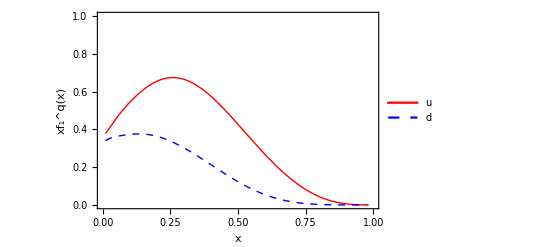

```mathematica
Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

```mathematica
(*Eq. 5.1a  skip x in front of the structure function*)
avPT[z_]:= avp+avk z^2;

(* Call your functions with "nnpss" such that you can compare with functions available in the package*)

FUUnnpss[pion_,x_,z_,Q2_,PT_] := ((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sbar[x,Q2]D1sbar[pion,z,Q2])Exp[(-PT^2/avPT[z])]/(π avPT[z])
```

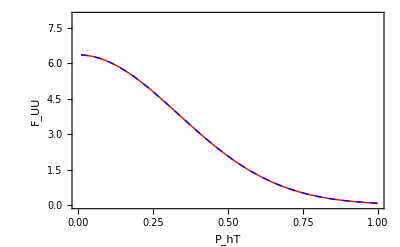

```mathematica
x=0.1;
z=0.3;
Q2=2.;

Plot[{FUU["pi+",x,z,Q2,PhT],FUUnnpss["pi+",x,z,Q2,PhT]},{PhT,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,8}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"P_hT","F_UU"},BaseStyle->{FontSize->12,FontFamily->"Arial"}]

Clear[x,z,Q2];
```

Phenomenology of leading twist double spin asymmetry A_LL

## F_LL analytical result:

```mathematica
Print["Eq(2.18 b) (*Cell[GraphicsData["PDF", "\<\
9E14ARda;S<:9LCUl^G[Yo>Pd<C62S@P<21_HVX:?3`P;daUKVMdJ20e830PDR0_
AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06MWD^c;CMeanOkDfb81o]F
:S_mOP`Hf0A`YIbZ^7aL6N0<S;4319_H@>b4hS_bKC;=KdUJJZUkMJ]kU`LnmmjS
U[@NooFDm>gmho^gmh[on[Uo=^=`Wk[j>Lggkkjlom_mVo/7KoNjN/kEG;]OdYnW
m]Vfdgg/Q^OHS_Ng[noon?HomJfn_geeonGmlOe_g]goXGYfmlNGgkfkEln67mkM
oognm/ogWkg]OK>^^fOG3o[AVomXNgLOOOcXgOg]MdNSVoiI]G6d;/V=_[6TgnZ:
o/P?KEdofo_SLoMS8l_ko]fmVEQUo;GoL;o?_k2EIW`>mlNO`/3Ym_SZcniOfMlg
n/<Go;?KJ?c27o@;lS/b8knn42Klf^gaQImI:=KFSOaBo48b<2kWbcQS9:e/PjU_
Sml_4ogJoId`h;ohZITL;n;@n:l9<I;UgPZLJ__a>CNmLR[@^P^Ln/n4DocNF7WA
2Cnf@oO/jiZagG<N0Y<7PlWE/jZZi_kfQBV0kLS`^DfFL1<93=oio1]fR;QD<WaO
hUY4OQ[F<]=i<Gkljn4n^ZYmSWdGmQ58/=k7KDMm>_AXJ^MTmDioo>XAeRLljmYN
V?HFE>TV6R@BLWm<kXMJa5Hhk_D/2<7m4GVKRI7kYB14]lOOg3368kC81Sml7gmK
A:8BkN3O4SWXhBCXh932ocPdcjV;610h>@H>==fHT4mQ@dK[c`XQ;G3C]Q]mCIOQ
m4Z19:YNe;Sh=oX[SU9]OALm_GWjA=6?Xn:64l4?a7AJ`KX2A8CYKnko>Hk]DbGK
eT8EN?Of^m^nB=KMm4@/kl<llolYT:D9E?ei@]?ZFEO3M4?0]dYFmlP>BSK<hg>/
i_2E:GcUddoMI`[:DHo]/hX;2NbM`bMnTRa46IXb]ikjImn/MU73O0c4kO7Cd^Ri
OZ8Lf8=A:H3LWk<3CEDmQfWBZ@n/b9I/CCDnYo4nX]Zc@8ncJWfHn2o_K]406D>1
k[X23[:a]EZ_:]Va=GS`i]@?3V_FROnJS;EXgC@Xh[;SC6@`ELUXHfKAoVKfPS90
HFo8MMWe<_QVC]dfP?RJclZZOeY66c;Jh6L8PS/I7NZ`jDRaI>X86JV4=Md<oX;M
QYCL7Sm>YPH0SRa9=dk?DBR@:U``9;nl?Cik=8;6P4TmOOkI^h299MgYVA=@6hKi
f@14WZa=<2bi5[>f@LcDUSTeI[H2HHMQO?JMbZ?Gh]_SXhoL7T/[2EZL;BCChR<`
2UZL3@iJO3nYaL?D?HNjEOJZK9CL^JS6fMaN;VnI<kRUFe3SPJf?KKmAhlF?=8H6
=@iSMMFZ3nODf9[hmSR]a]V>UEjHKTFOVk5/e;RJdD>AU;TkD6=KUe3SZNUDG<>^
MNZb6ToXXCWekG56SHLJ6OMRXR_G^A<m5T=Nd^=JH32SWb[b?E?TGn4FX=6WeKTN
@4WXdlk?JU3bjQYoWQP6]dCdgECW1W^6acSPnDjeORD2gQmonleW3oNYA:Fg[:iK
O?U^laEe_Q>m^VfMTkY[Wn0MBn3oEKB]JVU`=EG8;3PBehAeQoF_MN?_S`Ogn>]4
0Z_=nfGW2Vd/^inO<i[/USe6b^Vb?eUV=WBS7RB^1H]]/X/<a4ekWfZ?OBeHSZ70
;alDcj9;mNJnTW3><YOZDVER=0N[L=JUbPKWH7`4iLjU6^12ef5^_9UG2Dj4a/H7
mJWlg87c2X[Yj:fl:QQWe5O>WO>YMSRG@X/a;cX[:HYLFWGR58b=/OR1CTdLZiEJ
^]og4gfg^1cm/HaCB^]S7L<GNmI8n=2bPVILjeRjIG?ZESaG`=RHn_Kh<95dHm=P
`X@;:4[F3hX=jhQFTSOFF?a0]fb8?UaOM/nb2BjghWTSWi@iLmJ^^e5L=jaO]^/D
nEeZi_IX=>`ESli5a12D7d9<kGkh8QZ5Pb1=kD4eTB[CkBZ7=niMbAkP`@iMC::e
0@nl?A1/BU1UBoYX3o:_W0AF]@Lef=JYWeZ[URBbJP6[fX=/IQFHa78K0U>[>O1S
ELh=:gHo<0N/^ZdRhObZKho475PcZcW8EQf]L6X>2?PUa2jHPhY@Nm3laJhm<<<W
]@MNS0;>I<ki@O9:@na<1W=kL3CJf`=LTXKP9k<7^CFf5:hV[C3dH6^fl5YIWaP4
Lm]R4VI1VVbh`V/bfV1ODoO?VUQXb0A71OH_a`QGPa?SZ6=eegkRg5GMjUWC]<@a
;3ZC6ifhH4lH<oJbHBL[:^fjh`nBEE_TKUX4LD<_3cO50;lMWX=0:k[BhGmiCQ^L
/VR=nN_9P``Ek^mjdJTY<ZP558mThmg@<:WZaU_9OU9DJ06SG3`DG@_A28V_EY`m
A:cAk79DkWC=9Z47DQ8=XcMZ/K53Ih>AC<BmBI9ZA9YET8C]YF04OgIZkkgT;M@?
ENY/K8m;X6oiDb?=4gCY2K_8<0CmEm?caAonB2Qbd_CdZhmL/C`cHlTbKUgj<iIW
=K7:m3W3hcN^@Wg=k/RJUoS]V]UI4CcT5UMFib0UA:j_8BgLS`P1JF;?>=F/SmIA
R0Vo`NYhn@UO^6Qd<]VkJ7?8Cca[P?BbcIWabHLPmV6d8VQR<`a7Y@6oa5aU]5OT
;YT<2SFhU[Vhj;@YWVaec9VZQQFW>ZKCoSD1@F>X82j5ZIc=4LN:1Z>Y7NQWK5:8
B3995^ICjfc6f^UUdfZX[K[eXn=E=`>9J1Hm^>BWPTZ@l@:aZ9M@0=K1@C5E/;eL
kc_T3N7BB1HYTfTeT0F;8BE/X6@TedXfnV3AY/GX:N/:63^QSTIBJIeRTCEL8iM/
gJVE23GU<h7;UfL25n;3FYJ;jmh?^UaMkFWS@NIn5>=1f4JiA4WVhaJ<6nI3C1ZN
UTAL[XIh7<;ddi<Z`?8mElXmRLV397VAeikBNDc=9A7<D[@im>HkoUE`]L>mY170
kdW5caO<K/TV;6HZ[W[JQTmL1MJ<<ENA5E[<Y0H3@eCn4g0lc>h4X@S35N>BdBJd
^XYICcSG8Q5nI/Fh4[CjRUTHZjIHidEbHU[>0<R@gK4VcU?];R>k4l=9829iWYc[
4FKOol31GH7]?]f39i?aGGGZf97AM8mXDSFX:ReXNdR2T2ZBaM?4/:IO2[NF]3KT
TB]De5Yf>EG4F:Md;bbk6g6N0=`GU`eFe6@`nhf/GgKA9eAND2cSF`ZnBn7_:o1/
94/D8KHP4gF;Sd?1X:mM=Co`AVERPk=k2J:^`FoQ:cS[e9EE[h>G3]2B8WX=J><7
Gd5Jih:Z[;j0]1Qjd^Pm<K4T0EI8jhZJIi7FDcMlhR[BIZbiR[CHdA7UNAEY/hD[
hYe3FT9CDInGT=J?GB?5BJ@e9Wh1JC>^_hZd6OUDZdhR;M:[nJj;>4_VJIQY^=U]
TK3LJ@A52Vfm7ia9>bGla<KI63doQ`6/=3OlhC;J//cdAm2IdEoO;gPhh_V79Ao]
ee`c]CZY^_LK5KT<d2@hl>SbcM_h;8e]10oWlIU^c7VnMi=d_bQ;EI1>`g=CBHmC
=d_a@Ue6>Qg0=8XF;WgOWTnR[3ic;H_BcLfcad05fE@7k5PUG:/In9g?[4ZAQRiK
od_cmf6/2/U9WcfDLfGEe6cbEIo;ggN[EDLTFFEBjTXhHeKSB@IGm;MeA>MSK9V8
7_nEC4X@Xk2?RgHXUl6[MXR6/FQ3@h]L>Gf__CGi^RnI8F7Mf:[0ZKbMLoS3F9DI
WMO[RXoa]`;G18OOVSPg@bHXPH8CCNgiSUGQSmE4OOAlIUFCa6QKl1mlm4hJZM[3
7SMSbl5fQ<4[fe5<RA3AEZR5_NFbkIP9AekJ<WJWVV[V;FkIi=C0/RO/URWI:BSI
XgeQb]hdEEl=:Llf4nDOl/I73SRTnO_OG6/VLWg?R28QWiSI0=TnBDJohO_^^06Y
TcmQde[Y8/JFl:=[bHjMc[mbOh?5ffl0_nGW2=86l;/dP9?Hm?gO9?cfn[mI0;mf
LjLSF5;/ZdISO?glLkMJ?_COkPLn57n7mK^2N_aMoblLDhSKdEoi;_aZg5i/dXio
XklB?omjJgNiZCeb9f3Dd[hm;b9TiU9ZH6XFZe;CR1O;6P2=LghfW/E^MHHj8CiD
if1;HjAPhcPa8_Ve<gd1U8SGglP/M>PG<R[/m0Dd=F@PTMbA7Mgg:n2af=RM=WCR
C9;W7Dio[9M42g^^2IfdGTlGCj1Wh<MY4c^@ARM`kXQMIP9Y_`dofWF3:1cH_1c9
XU<fb4N[dOPGU@@DZae^gg>::QbA^]MaFYBFV^/GGk]S4eoO4HZV6OW3knnOL>iZ
ig18?N9GdTX^QdBZ>FaIYoeHYmdK?0f^?C0G`>1FW>VlmifPWCAfmi7a>W]RkLcB
TRCD98nEcjhF?QU]fDZTY:4FfB4dKM>5OIme;FR:9:lMaZZlnXW;UGelVIY5nhW3
H9fhE=TW1Mk;QQ7aEYTE_E70o534T0JhQIi]b>g`h^nBhBj?2D?/he2=71JRTB<W
_6NKe9]o41B^hH`dPIDclXd4LL@C0T3>PgHaka12V`8ObM1=dn18<Rdi4QD2cD_^
7HeZY7eGo8L<@EGSdbICd`6@Y5hT`dYg/26A6hJkQL=Bhd<;:lMhlTKQ2R<OaiXC
B`68HUnnK=DKlXMa]34cA`ljYcDPLJ_]I568U69kN44;56Uo:8H`SK6`ZRSgOlWD
e/9KNU;T`96=LTW]c<Pad0f<3l?@jCU3>@n_6lmh0LIU;PN<]`DH0BgHEP36U_E?
56Ll<8KYPX`oo[NdCk@K;=iZVX_Fge]6Vl3FRRm>9RIW[mGaI9ZBU^iGCRcZl22G
ZQ;7n]ABH^b1HQ^NSS]XFmYQ11DbI3<5Jb^E[GSRi;33h1DN7l>R[;TVMa=PLHg7
7bcD]/W56E4ifk?3[0@FJM6SFF8G5]/AJ7MH]7;77==ol6XIL_T2B0HEG1S3DW8T
33G]U7>VLTV6XhUP]/:SA;V<VNWF`_e0^dPMPPY[6YI@PJcSLn;XGbja1XjJlXhf
^X9j?U[Qk1Q81DT2kl7A/>L5AaLT]2SFXFR3B7/6oj[TF;437>eX>R>CDfKEU/dj
5433IXDeVhYR;QYa[nQ=N@f1>a:^SMSJe4UEDV>^oHhG58fo_`9A=PoQ2QSJLC8=
[akjRW=iP:5>/EaQb]ja]5;^:NQk?ehGCTndbffl5hff/c=hloTcN4S@A:FTAH>W
f?VhN`K?KGD[6=Qd=S[LFoYUjdR`81V4/U:1Pd59?M3h1ZGFN^[FgkPBRTe/0heL
RX3ZWZHJhEQ68MQ<Mb9M064k=M:P7oR^B_WAQEQ/E8869E54nHT:jUiP4X:RUWAi
SGogBRc6g=UXEI8HRgf;QnX>RLHH[2G5gg?0MG4e;/EP;CF8]UH@doW>1V6ij5d?
`[00dZdCXVnM?C4j9WI[49K?O/kIJ0102L94g?]N4iHZK:Gl[Po2`UQMm[DP;1n/
4amk6`fmcA:41N5NXoOk1LV<@MR6g4H@APbejfeX49HCg[?=1F4T[fSd?AN1hGga
7APQ::lW][a_WFOh]gPSdE]71==:WbZ9Q20o:P69if3;3a7HA2]L_PgElc<Af0A>
QM616BZkaii30eB?^9bbl8[kAOc25JG>Q60SiJAlgC[cL@SFL/:=<Ve;<HScPV/9
BRQVnj_hF]979?N9c;6PMCh2XenBHb`f]_eRTMjM2:agHR9M=H5PQa5HV<_3HQ:1
DMbVG5c`7^@FVhYO2k0HiP/BOR84`c6D;<e6dDk6H0CX>1diOlo:ID^OIlDYZe`^
EBLBC3ELlIIL?GERALF`K@FWDPQ6RXOc@CV`VJkUEY=K3RA8Ij@=alNXf98jWAbi
DY<O?IMb34I<S^7LHMJE64b^MMYCbaml>g8Q1R>=BoG>`/9kMQN0iJZ:FTW/WC=N
HJ4DPm5EBWPIL24`?]:`Q0]M=D^K[DhMQQ/BJn9`Agm1Ab]f;^njl6<TkKP=Rhdc
eR5Y0;@5BIL`bR9IAo]J9hRD^lh^j;g9QEQ7@AQeah6TOiUIFg7_M:`gG5MQF4YZ
dXGj6Pa;I3AbcIT=`coCCBl^IQb`MS5YFj62FH3B3_DT?J=@^[:CJCJ[48WQ:0`L
DUcde?GdZIP@RZgRTa>QV5bST:^;aV9IiG>F:^BUTd/Q8Z=K^6XdFJh[gAC7BQ4I
GTk;4C?eKYJnVoF>]h8VQfIMA9IoHhW8UVC_GW4<2/T]J?5bUj@ALU6?hn:HSlP@
>jkN2m]@3Ogdg>D^[SZ6WVH4EG`i7I5QI42Z39g>E/NH>a^]c3b:b7XiL36l795Q
ao]>fiee_]<AVJND2/gi2jUlFJc5=IIk]Ej=b;;IcoTN<B9c9AUEV/GgF8A]:nH=
OH=B5V_mF5gfaHP/6j`C7o/N<B;c`[d6l[<AfIKLATAfU?n=4EU6N2ld=eLD:nE^
G30/D:g>]FYXd[]YF^n6:A/9BXfYG@ahH4<Kl]l=H]IBBZ>?<Y1_hmJK2N^6a_RF
f4UBl6g/d3[]/W3fbmemURmK8BD9o^a=TejJg<8M`PN1DbDmMUVJRO8EMfK9`Y]N
=jgTCYd>bfEYIU15g7^3g;O7lITgJ_BTCQT:VjlO0I>ZE4/=Ebjf93/@V:DD:iOO
i00=a/B0dM/S2Oj//8AVTdiL2:hdJ?M_k5Pbae8YM9=i2;hNoM4D81cb49aamgHZ
nY<ShE^U?Qom@NF<_d[UA2k]05f2?aYn`nS0Xg<0k88o4YHiR2X>UX<onZQGHh<b
LZ>L>YFV9X]8S29H9_8O0k0;oVAXjUc4NOfiY_gSU2fifPhGMXMEBNa7nhoP[nBL
;JfDFeYk:/<iea@?l_ZKOK=<2bXd4T:m08D]_C2E^;8I52ZRO5BXj;MDm=/MA;To
BW6Sa9a2O`LYJo^Gl]dRVmC^Y2<U9i]DVigmBi<EiW2:M`>m2?U`YKZR/5g_U2XD
9j8LcD3QX>=:/a8:BoG>1KaNBl>nMNIdm=IITA;Li>S]S5jHNC5jRd]n==H`NRDm
hcHeeg8Ja2@/F[NLf7UCa3^f:TU7SoiQeAjGKXlBnWM8IXm[HJ5ohRBT<FLH/7JR
CaKoY>LD>39mj2/a9fE]:FQ5MkP@LiYB6Vi]bZEd^D=LKZ1`3JB=JcJU]GAkJa?]
V8Bco=?IFi]Vd^4]YG`l/iE`K/;?@VmVBkM=_a`heV<O5gXcIBGI=bj6We@VJmXC
@bbR1RUE/^>28;fIm=a@gJ:YIZgX9blGeOPcXjPJiM?a9dgbg7NfDQfh7SeTBgaZ
eid9AVJS5FZ>hTnY/b>l[eH4YNMYe?I4WNmdo>TYYDbk77mbcd5bHTIWC`b2jIIc
/_gIRcg?Ien`mISD/J2H/OVLmaC3EkVQ==kEYL9jk3g5l3DK6kfHe8Y^CH8LbgHf
e0l>fZhC7g]?<Gc=M2?6D:O3Ei]KRO]DJ5n:hF_6=nGj3i@CUo3E=^L=B2nWVeXi
ZaI3Q;>f3@N0:l1aOC?6jo`O9QYZd9lhE6hfKX6Y<IiAFTC^b9cSl=6::MPTnG=E
5QFhU>lF<S@dOG6jN;GZdkejg:e4hH<Xab3jkJ7NTnf]=ZB2FnTiHN5MK79@LZO@
K2jLJmE`mWGVUH4ZaK1/F/Y<<5XjcS@[6W;f9IZi`YhDRfQ4UVi@?ebA?75SC7aY
YOhYZG<CRhmMiEKJM2AO8JkSoX<@JA2[TjeaO=e4JZnEIX5IJ/`Nal=>EJIC7lQR
TDPcM`:bFPO4PDGQi=gmlEjR4^I`KV=3X7?A2Y:IEoG=dEbMd0eA?/;BEBeB8k1E
Ao6b1ZO:=Ph_5/0J:agM/2R3dY<hg883CYLc4?LhW1oL/bHV3`Ji;1Rn?lXEC2B;
0kXk_4YP>4BaNlge;IM]CIWi57MGABJ_H=Zh857/:76`0HHig`dR<9HlGXJ5RRRU
h4ARf76>0[M2U6?5U0M>Y=_jADBA1T=a/g9IEdA94SJVU/[1XlWI;NN[[kCd68@k
R3a9d/F3L=RdTZ`4`_;/RZC<COA?1flieG5OAbdC6ec>jm@7Hig9DeaAgDkQfaX[
5bJ^c:G^]iCVh<DUWbl^8Om>m8^@L4ET@?jEP2e5Dlb@kl^C6ZdO/4;_MM7D5P^i
gY5kdL[PGBZJdVD/nITM67niJ9XiBWKAm=OGRjI]emhK6/4hDk^Rl2IZgBfJ8]DL
eN3>@011SfZTUaFT_Z@=H_CN^<;fjQ]WXeIaa`LF8=dP6Vk6X^TWRN4/5De91O9X
4@O=<6ONCe5Iom@ORTjJLBdcFXNX=JNX8]?IZ;G1FI/h4I9jB^N[Y_UX=BD7DF]3
5d^31GTaJQFWU]NdE];cLD9eTe;Q<66PE=S[iCiF>OHcaJKSj2bU3X/e^hJMnN`:
RLUXXcBRHJN8fcbmESD=HgGGO^;KXo0620PPHFLnf0XkcBgS@3M@:U1<cH3:agVG
ABi4U7]25mYU;X]_QTcdI6]D:7aja22T4ALReKCK`b_JOPFQT@NX:6/]ll/3IkZ?
a?4`NQZUnXUZBb`Ukh_iRDe_db@Q9HN1mHJIUHA;h;Uh^^I`FYjhYUV7QmWm`X_A
7a3MLkkGEC9S@hF2DnXkF3=;2jXl3i8_G4VFS]hbB`Yk5EUXTfKinEMcJV:`PA>4
/XB1XbPYY]gC9;IYU9da9Sb`<Ne3aIPTPY?@b`e`V;JD8DlU/E/iH/mAQP1Y:`jE
0cQYdLE7/c4Y2N3<_MHLeJa83SBBOeM2WDl]B5f7gVRAL6Xl@CK?8YX48E2Idn5;
fUN1YI188bTP<EPn=ZYDVV[MbQH?gi2E@2kma67A>W4YT@H<h<Hg=:W9na2I;]nF
26jASDI9A=6cXaXDkAeKX;noe5DWelC8<FMi7@`<38]Efii^e=83^FQMcQi;1ZV>
3l05PgEkG85O>CKBi6:RZ/aIK4Un7J<_QM^9Z4m`E6iJC=6G=b5EYcih<jFDjXIL
BV1?7aGB;3YSODP0@@::cg0n4=12Cd=B:1_gPYf^nQMm?3FLJA1SDYmkPi7AE;>D
LDVhJ8HQP[Qbf=4?3X]FNQm7RhfkbHP=4iP/UjL^X;gT:LdeP`Nc@7jjJYfhU;6C
9a9OXkBP5nY[4U[:WL^R]eaZJDZVF[TJ[1]>A<^TM2/gP^2oLc^eW;UI:ERB:;A7
TlVIdF81@1EZYMH_SUO]BVD<97e5R]C[`dH/5abAW96KbN?8HV?T8[hC1ad0_HYl
J<2AZdJ6mU:fV4^5IBD:nGn2NUh3FUTKYIMLjK30R9gnUk[b@4]Cd>Hm/YU84<Mj
K@jL?RdW<6XD1g2[6:GKINE`RM`]m]:R^LIkhW[HX1UQdM7BUB18CP_:>cSIZSd8
gAhU46[10P;JK:`bjaR3^PYY`id86;@RMN[jFAQ4@b[B]T=ZknW_gJXVYja7/Uf_
T;[3e0h>LjGGCo_eC59_@DS>=TbBeLQ<QAN^LW@QKBHEakD220FaEV>AP91Y7C^/
O4M5bP:Q938aXTYYDI5H::1@h=<12/FYe]j<M>iU5ek/[1BOSfZ<QD;g[>6^T>hR
UY>kWX=OXeZQ`[Tm8f2:FNSGb>CkaGJ=DgOE2he``/CoW3^e=;[VCN9[]ef3d@8V
h][A:jTNJ3P]L;9M8bBnlVmLC7aAoiR1Qk00mIoca9Llo;5gOY^ZY>@E/;lmBYHk
Q9^7?dc[6a=O6DEEKDhW_RAAS<_SEj3PF7:]]EfSbDH[=hlBGaQn>G<K0`4Pjl8U
FPfoc[/0@NAe_]>9;dlYIM[EMXf6ldaTaWFhcYjT[TbeegJ=8?TjO8<cV6e;DF?N
;6?cfBSCWonFBbliXABVEV4]A9VhG7;J81lK3L;9_9VO>?1;9djSC7?;8FmV4_aJ
h1KbIQWSUG6Dn/ZAVk/n6A_1WC/La0hD==`VToDBkm4?V7=NYclfCV;>^>o6CD`i
Gd5NnEibOJCaGbi:b:MFmBki?Pf=oaggm>FSMN69mf?UnjC02JFTH`NHF56/i?e8
hklLk``c[a@m7Kge@]Y:;]RGVNGPX<hL9?I<fXck6O0SZ1QFI6IB@3bA=B?AdO=j
RPf8A^E<VRcL00n8BdBc[YbIX22W56[9ZWXl38_e33[A^bnZ;@6=3FQW/fJeG:92
n9MCZRQK8BDT/3R=:]PZe`VH6QjK_<7T/VIhf4]KS<9:0LldJiJ=SGRFF[b]J8Th
^ZbI7gb0IlIH5ReI/iYRGALK8j=Ha[j79M[E[5U=UHSTCKBEei9Vg3E2]:S54_D;
dWfJf:]9<mj/BQYREKB^9leb:E4<XM_]1?Kja_NJ^g:4P;VCU:@fM[2GHnKTf^ci
?eabKYJLT@jAfeJ5IL>TcZYU/@efbh^T74kQe:eDN<>Z8k_;`<fDCUYBiC:c3BKk
Z?4=i:C]GBO8KNeJKXVQMl^]G3aGMdfTf[XDNlfIdNNA19PeLoW85^XUNoCd3S@k
AnnFaQKY00_d?S:DFfH92T_j?FOFfL1ENVUJ:Am`hXbP9<O1D]`ZWG;bj8Qc3dUQ
nM6Z7lO>PGBJbj=k3AJ?Y6?HlhIN2j8/TnF8LRi`IHmDZb6B0iCEBX/U6VZGTn>]
4nR`EXFSe5[h`dNkKE_RRHUdAZ^CeD2ckUVkhl5MPDQIcI:bH]^FG9lXHc>]E]e8
/<PfejCQi@6Q/?I00nGe<AKaa:fk]=EJ]K@Q7BJ7bL7Gm8OTZhhf[hA5L^9:O9Al
fAK[;41XJJWXB:l/35^:aZGJ:iT2h^>PUo6n92Eg2H[TXPhNm]FIEn@^iM0P6Hkc
:nBFnc7Ud[hCi=i2TMcAR:GC`F7A^^FBQ7EL;Mm8PWH;ABO>;I7<V>SV]j4X>KEZ
^?]h=>iVZ`15Nm2m@95L;n/W4bQJo=icVGc95DjPYHE5^N=KbZ59hH1LW>GVd?Uk
nL[3l?aH;^aP9ZMQEbl4c`SPYNO70;a>38FD0F]eAQ@l=YTcISA_39@[/HC7d/2k
M>oX@BOg_Xgg3@l[VCEFBa9`ZlnPJk;Ak?HNhjX=@/:IOSmN_dh>4LB^/DB]3D6[
/GWBJYS?[3K?]oS]9LKU0CM^G=Ba@KL48MaQiCCX<5I=VUQ>4<RZYH?F6nZ`j^;k
=Ya6U?<BnJXS0Ymng`KWR^LkT06DQZA<kYY]6^E<QeScQD6>`SLDcLoV2kT7V:Bi
BZ6>;TDEVRl<Xl?LGXI_SbEO61];mM;m6[]Kl`QVS86@_`_i`YZBfmbnVRo<:GFi
DJjFjhZ918;0n=eVWL<VWbCjTc?Bg5cW3ROhhNL3I0k0lS@11IUNGGP/TY?cdXF?
F4e<B1R[boHCikf@Fn/U>ANi=3`O[1>W2Cn7bc/_C4QlGi6W55DKUXHLgC/_N2He
d^B9QXETCUXFXg8fHYJ;2X4B;bfII^@K]o`LPTcBCT8gTme9a5bX3cL0cB0XiH4n
Da9oignY@=c@2m]@a:_9>hhaDggFQfSTZWn19]?@77^YDT<KZEX:inIhH4WAnMQ;
UBJERChMNHE/boBBTh[GPnNc=Xl:C6UlHC:?g49=niU5li:C:TfQ_9KReRgmMSTX
9mK<SPW4Dn?l/Tg]D[<9kA[dPki2KJhOYJg7[oZHfU/]UkCSb4hmYbjjZ7860m>5
ln4^`?ODlW`Z^jP^e2JgJaV@NgZaR^4ib46WVOjYFV@d7T1LI3>dT7hKSLlbf@Y>
c_VXg=N3X`IW<cSal9okZ9I4]X82S/K>gL_0j9if;AC@a5dF0P2o32Ibe</iS;I6
;hfgQYb4XDjQ[hZ9Jdbd5ek/=A4_G?1_1hD>eda172^FbgIde4XX9?Mi3a:`I^BF
]<Ni>ck`cZGG>1o^ANHNCjWJGD7LJ>UNWA6U_0i3GDgAQ3>^=PbEHVG0DoC:UY2S
c8BdZTSKKaWc]m8U;`;@e_`B2<UMV=b5b9YO@B69/ROZHSH:9CTk0hFjS_`GgEnW
DFRIK8e2jfhCdki8H4j7b8/Xa3=6[S5`ajTYUHPT3C69C`@DRWBUH9n1V;Wd1UbD
@e9QM00@o[b9e[K28AFaGU9]/6XinPc3P`Ml99CBSC6:TLW6APa8PaaSH[Hjdi`G
1XM5jlBY1fb<IM4eEg7E8]WKb^E?Tf:5IC:T6lJUAQ6a:_Iba9<iEca@Kb5c]RT<
iALlfF3Db1Dh9>aZUXCm2hcWcfMHAiLdCb@j:/bMm]<SA6i/:@<VgZ_`;Y<h_oAK
hGhWLD3UX0@YFW8T^^S8m`CkkH2=<bXSa`ocZ@DH=i/f^BMWE;SG:YMf9GZYI<<A
3c5hhU]aUWc]PRkBK/i<Rn<P^V;@k5jh65QjUVNIfC<jR;^eijfhak6/6TJ7E@Mj
ihEjHc0kZAdhY8??BXVhMQ:CeeCiJID<bnK?SUE9cLH49RVSc3:gM2aBRo3TER6;
4E;RBNX0G53YiXQYS7=WHeR/93mZj_Ge/3k^UaINSY>MLYbg4VR:n52hh>W4YL9b
Kdd^/BR^435oCWDVT=Umbe_DGLhWfKO=bO<1D^c7^iPJgO`bbMnh;H[KRWWj=7/0
kn?o1j=D7ad:IFiTLgAbIF5]2VE^I6mRJPXe830PKf9Z2STb>C0:IFiTKf9Z2S8P
<21_HVX:?3`P;eAiL6DP;e1QIfDP;e1QLVE^M20c830PDR0_DVEcKgEbHfEc83HP
<21B82m3KfidIFidLb0d830PDR0_CFETJF52KgPPFc0P<20e>CD^<SLf83Pd<Bhh
>Ed:;d=bKg12KgPPFc4d<bha>C@a83He=Rhb=c8b83Db=Bhf>3Da83Hh=bhc>CEM
82m2K6EUI49_N21K<20`83Di=Bhb=cHP>3@a;SPiG@X_E79YKD9_N21K<20`83Di
=Bhb=cHP>3@a;SPiGB0_@G9d@Vmh85/`830P=CTe;S8g=R0h=34^>3UM82mBKgAQ
M6DP<20n?PYUKVA_HVX:=R0`86mRJPXl?20_D79_He=UM21K82m@A4HP;eAUN7@P
GB0_AVm^M20l?20_E7Te834a830PDR0_E7Tf834b830PDR0_E7Tg834c830PDR0_
E7Th2S4d830PDR0_E7Ta=20b<20`858P;eAi<CDP<S4P<21B82mDNC8P>20`858P
;eAi<b0i830PDR0_E7Ta83LP<21B82mDNC4`834f830PDPX_E7Ta=R0b<R0`858P
;eAi>B0a=B0`858P;eAi<C8P<CPP<21B82mDNC@P<C0P<21B82mDNC4c834i830P
DR0n?R0n?PYUKVA_HVX:<b0`86mRJPXl?20_E7U`IB0_D65WIG<P;deUI6UQ@Vmh
85/`830P=S4b83Li<UdP;d=_MFid834P;d]YI7<PFb0b830PDR1M83hn2VE^I6mR
JPXb<b0`86mRJPXl?20_E7U`IB0_@f5dHFa_Ib0_D65WIG<P<b0`858P?Sh:IFiT
Kf9Z2SPP<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAiL6Da82m2HG=U
AVm^M20_DTAFE55C:d==CDTa<20_AVm^M4AULf=bJG1dKg8P<S@P<21B2Rm5KV=_
I6U^Ib0_CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b83@f82m<HG=d@fQQLR0a
<S8P;eMYI7AXLb1K838g=b0`830:<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<20h<SLP=c<h83Hd<b0g>3HP>3<a830P<20`830P>CL`830P<0X`
83Li<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`83@f=B0d
>3TP=3Lf83Dg=R0`830P<20`830P<20`2S0P<20d=C4P<20`830P<20`83Dg<B0`
83@f=B1M83hn2VE^I6mRJPXb=20`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1d
Kg8P;dI_KWA>HFeU82mBA5IDDE<[@de=BC4`82m6K65WLb0c<R0_AVm^M492KgPP
Fbdf<b0]<SPa834`=cTP=cPaG@X_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P=cD`
82m4IG=SIFid82db=C0P;d=QL4QUJFMXM20]<c8d<SDP;e=dIFeF83Lb82mHB6EY
IfQd2Rdc<SDd<20_DgAUKDPP<c4P;deQN5MYI7AX834a=38P;dI_KWA6JFaU838e
830PDR0n?PYUKVA_HVX:<SDP<21_HVX:?3`P;daUKVMdJ20b=R0`858P;daUKVMd
J34P<SLP<21B82m<IFiWM6Pb838h830PDR0_C6E^IgAX<b0b>B0`858P;dIYK7AU
LPX_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1S;]UF9@;fcI:YgA;3BWMSGBgM3M3
`m3MgMgMBTVWM9NDQ7@SgI82Nec[NIK[OOONaoOmPCV_kW^H>J0Rnj3::686<P5:
P^aM65VIF?P0HPX:<Z`/01HFMRHF5SHT:RXe:aMKh7oYB5@J@2MW:i0mgklTa9b0
aRiPV[Ra2eQ@0F@?T7Fe1K2b0eRin5RinEQH06`/;;aPDgl9PYch0>;6KUIV00DV
P2c87^R<A2D6L_1d/[:`M07knNm;08dY;H2EUiNKhBmeP8PMd<W:e=PNX63/HPVd
0g/d=KH5Z89<[H0^W_o31<ekBaLG1ciVIWMgMbIS>fLVT9>582d3`=g:aA:P0W@6
>[T1c@2oD`HX6]/1oi<b4a8E@<gBb_U_QR[8g<GMf0T801=/[Db1m/iP5EMk<j0C
0>`MX2XS3e1b0=[o;Bco]`03h3o50K0b/OiSkSoJ_`eIfOnUK6aZ2[9c<;Kg];:g
09QKf@81BY;bC2hN;P`0Hg^cgh;6]/hPL3S6K/IF]/HVH86o@SL6B8XX0hc1AOY?
O/jVCUH>;/i<cUJf_g=ToVd6G6H9Nc<aT9dMd=k56NUgU^9FCT1C5i2C9o=oVV]S
3g:gmoh_<[Nb=c?oG@`cE`MVMG/[AeNPS3SPKaT`2NT?c@;X0^1ThN5Vin4401d1
@0mCBnKO3]@l7H20gdcFgfA`3[kN3R07P3Th3J2_UCT@o0_9fmWH3@Q`LG85nW[o
Vo4o4A8[:l3<b]@5H0:d/;97nV<MC0JJohg1oGNblP3X/X07U1D07UG0WeOjh54d
0mWKN_hAoj_5c79bRQmTaNWoDh1oK8V:PS`0gXc/K016=ThF02/;1`n06oc2mgoJ
nF1/mIl/FOhHU[4g1h4eoXhGG:Soa^cfmhH0J?jc@kB0ofU<4@@NGB20i/nTjk5`
/YR2Ok3nGllkh;O:omNHokKbOicdoafAY:^]kEmUX_Vk?_l__[6MUJgWObC0Xn_Z
0Uh31A1h6Nco]jPVl?LJ0fPDP6IF[WKoVb_SHPaN1a5k2o18<k9b<;5`o5e>:fM9
:`nPf@L[5e?;_lOVKk[jkhFc]K87OP0iFodn<F0]l3WiZggol<1;JfX3?R?>h=Wl
VfG/35iHUklJnE/D25jZomT22G]CT=W_kF?Si08H>cTINb:1V`m6W01_E_2JVP4m
oYY^03>C?LP5K0<0c]TGH0ib@_[MJ2i>0;?8Km;OR0_0;?X7L@>HaOhP7P2cn1o4
2f2Fn0Ma/`2H9OlPEP2ce1o41V2FoX?07^Co8;07QCl8k47a7l@3]_WQ3`;KE?j3
`3IEoR1f0;?Z7l@1H5KkPl3iZOm1H>lJOa3H^nHO1?J^m@N1lm?n1o62Hm7iPl1j
a_lPl9Xc6m/jF?jQl88]VOcQPf<e0K[lR`dfKOX?Vo<g0Ynh?ocOHl5/mXl0:cPO
<j3]_`b`PVl5<o0O0GJ`0=01O3S1<oGOA[:2doh?SOD?T@DLbUomoj_I[2cP^UWl
hOi6a_l>Q0//KP6N]]l[lXmQl9`cFoh;PQeIo@^22fcm;`R^U<doT0fLUhfaPl>o
D`FGb_J?03P_Ff<k4k<o4UaP7M_O2o7O07S17VcoOU[l@f=U0AOAkQo81XkKc_DO
b0XnK<aoB/<>cQ=T1kChhh>E5JcPl8ll9cPV1o036_BW1naP2`jFOo9T0fO]l0N2
Kbhc^07oF605_f5PM_`G1=O/C`WI`1ThFH;nHK>1RnA/IO6_2N02el7Ie]SiGgEV
1B^io:?2bP[FnEN6_dfjoOEPo9L8^2K^On3_hW_l0mW04GWl:f0f/4O?OkR/_b_X
mAOlocTfZRkPAj>aTmToenOgLC9eMG827j^o7W[P@oEOo=OK0R3@0fR:];@0<^D?
/Jh?jKR_5B5dImbKO0mkWW6_aLHhFF:0h38X<F^hUJBJVk</Eb6i=<0ZJF3M[BSZ
N9ng_WS]_M]0f^S9LL]8:WUP@FZB/?1j2cVGk7e7A;j0ePYAZ9TVB/;gdFT@hP=a
=7X?XY2IaJ0Z5I[?^o[nklW^e=RO9;UU@c/D^gYZ?nG8ha;aJYa/ZkRdVHbXkG7N
h;o;gkJ;3mj9dH]<El`RUg_OmH2Di5j3_STl=[::<D3L6adXjaJdMd4IiX8Q`Cm2
9<h1Gj>aFXCj:onSfg4FY[N959K`/MUPi@I]fWfmhYGUk]Fa?QU=BPngYE6:N@c[
RML3<HK3:[IXQU=1lGjDfDYN>2Udbk1PlYfcAWnVUGCON_Df/He/N:RLio9LolcV
;eNiM1WMZJ4@6PJ5986GZ]dCgbJZcUPglc2XmWNeJARk4_Bh>KA7_^K1AD>D][V[
]cBQLiY/^S`IUQeZPVF[_27]0EXHk>`XKUHIWmEAVI]n3<>GJ]mjNg6l55egMHUB
;c_FA=_7H/IhKCJ/nVBE53jN/c:?=YYVe/F8NKWKKMgje7Q/jL/?fh5:OJ^m>^`h
CcLG<N9R@7`0d[cbXnjXT5QlY_I8l^ZEWH68WbAED0UV49lD2bXOK`9a_`j1>R3H
TM`n1LHl7W/m7d=U0ABA71ZmH2/nh?1[c7IKL0dG3B932Bha_5h:]ZL[1LQbf8V`
C3b[/3L_]=5QSgQgdAOQ]^mRlV9/QEZikTdYY>`Z2J=InS9R[M34X@AQ:hl47bK5
agB8K=jdiDOCOZ/SW3]mdo598121RKOlAlka3K/5hM_[705DD]d^@m9GTeN@8Lj5
:956bLKSD=0hO?>E9SWY:@7DKW=^M]nVlMDQB4OBFBVA=RBUQ>[LS>fZcCe6lD_e
=fW1Wn:n?bl@EW8C1kECDC]>6n]H[GDn1e]l@XG[ISGYJ/^A[C3f<NZbS?eXhToK
jjhMO6jZBleRWG9A[`G1kGU_PHBEHDVPfQ9JA0g[kh_Yl<8hNfBnH00`OUX`A1XT
]>G`dSRl?[1G^Mk/9SJ<1@[G==11NOVT9JIZFS6el4k@aPeWIX^6ZLI]>;=?aLOK
530Ha9PTIEehSKLQ62>?Qg8HR/;]7671HZhn3Ddn/YkCcbaSO8=4>m5/ZVLKL`3U
R3oUE4I2MgT8SYT_BSLljY;ZZdWLmUYWZHa4nC7C?b7_k^8N0K8bd=M/NGJm]5JC
7>Y_l[=cYLTdkUH3cI[9VP?hcCR:R]E:dIHhnAQf7]f`:DcUh^UF5oSY_JI`h;ER
JS2mD6`0N2G:gcKL1`F=7HM<^?IHHfDNfbKUd:U3QH3ClgN90Q57iVg=kbn/iGk5
OJ>dJKFmGJLb_;6Se4O?i=eQ70P^f<>c<IHOmgnknY2Q=_F1eG/j4>/]]We1I=al
W^Bb]hUJidB7>EcHmVU1]GNTo>`aMDA?3m:HERk_cUSIi^?MFM>6X50Pe_9^Xe[1
ma7@VHYke[L]?ZA`TVaPfcTBlaERI?/1<E4_?ZkWdfT[ZVm8@KS;o[9FDG0k>GO0
UJ=;b:KiXfl?i_i<2Ve]60n<Z/Xg[EA??<cg>Lj=K=JYBPHMFl7]j5@mKn;ELm]3
=kd5if:I2jYZb/G/@1]k;9=DEKj53R]hISnl;G4i1:<`Xn0=g<G;;XB1bSMVZ0?@
AlIFI]Xc1Y_2gDe220i_[=SiRNX3A@OKA8R1CdlT`cLogd3?T5O;VAk^6b8Qg@Sn
6_fU1YXA::4S`VXM7God;0UHXW30PZ?<E9lT<Rh;Z0o8iEAVdf7W`lm]8Aai[bde
hlejofZZ8D=@2le5HnRT@7hOjA9Z5Q0@_5JQN1c6YVmZIKaebg7m:W1>o=DYlh^K
idZ=Y@5M[kCLDYf?g/egkDQg[:Jg2/O5k0adC@=AKYbnC1FU_6Eh]OWTG<HMSARX
@>g3;=l4J:ib=UniH9Hc@heJg<T_<O0[4l`O^G[laR=I[Va4Tb:6GVc?1=fCe[F>
gVm;JlOF3/5h^65fH_T6k4XbDVJCIi]PTm4dNMV8:j^H^?0g3:<NFYNd3^CJ8>lZ
4]abE7n3hgS8_=UXF7fe5Z7;=[:H3EN^Z:]7Y2Wk`ClNF:^<XThJ8^IPL_1EV?nn
G`b25gQ8;JU;4heDm2_d8N6QC6PB?mH98^XdXj?Ml>Ic:3c6[;TBP^Kj==C>Yoa?
[Pl/JgN9/CK<BInYJcQo_QVMoOC@=?lM<K2>LD=NFd>W`^B4@b]?Mh;5ML8JEe1R
cZHnX9i<Jk17?Z6[nKi`>54m_OHfN`NP46kkZ2I==68onn:I?@1D7aYjoNDL:P:c
VQ<52VDWWOCA9`GDj6O^kQ=j]@F^:GjVCWfK8SF_cR[L5<K4c0_5?c`S0gTd9NVE
@UWF5J3nWET>2]YfdIc;`g6cP1SA4jWNgKL^B5ZJ^H6>jW759=DV^NJGMYdWb6>j
fO[cFKY7LKeZI`JdWVLC[CfND7^NaT6@K3<1b@<L?NT8XHeaJ84^[]OZQ7U6G@1V
nZ:i3=fJ[SV109@29Rkk=eZZS/_bcnS9SQFOViEXH;_e67G8HPQ8lXiUni6TJHVL
U6lCVXRE>Fn;oMG`CNAmV@DW>Fd`Co3_19CMRiAN^74iOdE@4?:U;S8DZA_RbWl@
BV`J7/=C5?^l[jY`>fme?Xnb;9R:RS4dMANamfK_TYe^dIY2/cmGo8SW89[bjY_?
EAiIRfCDa]Q4E>_;fl=UnFAn@glT<nDdFAW:i_JdO^dAV^oh^7HZSPMHMlFb^_Q9
O^H;j=2l36VEG0gKN8J/SlGOo=`1b5n>bhUD6F25F>>5PQ6@[aM4iPHg?6eYPWKT
8M^VG;hDT4:OZbMPWYdL8?H@E=X9cm;Q?RFXHO<V[4Rd@IEZ:UT`;ZL]m<JPeDXO
>^cSXaY;`i6@8nQiUCcgXC??OR<9TK3FP?G>IHflIYd8EZ];eI1oW^Gde9Ccl@ZH
_Mi9_o1IKWJ1;k4F=C/<eA3hk;G4_]bS]R3[ek6_FmoEm3;?K_C/E_3RH>lD[?i6
@D>c8_^Fj@NF=Z?;@FK6HFee?I]Gk_aUHTPYA3SBNeD^5mHVfh4eXblVFO]A4?W]
43;7^3?4Q[Bi>YWGLhI0M0UDEANDDWECcY>_HU_2dD6P@DkdH@milJoM8QUAcOk?
PhYUa=<Z203ij=<Llb6?OCIaV[BP2O^2n^F5W1F[eMR:ZIWb66NDoZF>f>3]AbJW
MHAJJ99[2MebA^RZiiJCWjP7`Il2_C[Cm^:M?/>R7Fg>DYJ:ER3;@c579OcPJaG5
o@UHF5nT3Y0Rc9^MI7GUH]5g=PY4B[Y9mLUZCjJY`nG8goQ8LgPQF_o<R67ClJD]
KbS=YWC[i^V;7<UW^nPehGG34Y5gnh/m>^gONS0A62QEP8QfLn:jd=Fa?K4>O^<G
WblRTN6dEY=5WWW/A;bFO_k8PC7[D^@Wglgd`hNKBO[DiK3ALI^>ddXP9UF66Y2/
>9eO6cN`hL<?T8<ohd;_4MVhVa/f<][]/^ISAXK2Pm1YR0mhOE4_Xj9ki2;DngkM
;;ZoUKbLn7k/J>m33:D3]7Ee@<o@XG^oBbRmeJMeZllU/QEcNBfoiP2MjZF3haO>
1m[]^MJQ_TE8NWd^dV97l>MS3bBIc4SRFg^0;f>8gUK0PIdgVM1Ek`][2;^>YYim
nYRldde[`fg_FN::8fPnhRkkRb5Td9mm9FXUF]9YOG6P151OXQ]oA6^TU:Q8TYB>
]H>PgL1K;f67[G;ID=Vcb[JUI:7b/25k5/_T2n0mo64hbOS5elI?OTKhafUE7lZh
U<20@JGUmb=JVi[/=R]47Y=_ROO2cPIhmaiB[db9H@QXaoQ:Mf5I>]5WeSDkT]QZ
ZagC:0bDa^O1KeEFJQnMcE<JRd^njmT5V=Z`P^[XmodA`ROf=f02NRF>`Tg>XaW4
?S]Nme>7?F]Q7L/DI`o=IL0hMNZ]=?L5SKi^?jT0@DI^BE_]CVIh3T8WDg>OJg;<
ilDVLN3ZbQOJ=65_7L;V[VgPRX8WAd@:B=5YU_@EMPTF<M0@dK5_Ea<<0Z]WiYEB
jfcGYZHm1HQ^?QUhLD[4119hDKh4SI^N[[><fjQ6>LAgRUa0FGidLTH>kH``PYGm
V_aR4mgA=R4UHCU7OB244a`::<KJo4aXU9Zk8l`KCIH1dQ>FCcIFBmMGLD4n@O?Z
[WWgUZkgCYdoS55Ri^eNJ3;XRi[9mUXgifi=BoN_C[JD;/7:4cT?AoKnd/eA@iN?
a=GIQ`WC?S>JRe@A;<DC0_/BRL8ekBU<if`6Vdh=YGci=<CBPUG0PnD?4f/=Lo`e
Mmn75`]3O>ddL`hI;i/D]T@V_Ib=W4el4o9RUYkkWE^5/@fCWC^HXM;cMR@S^T?@
U98TnR[CKLnRebgeY8a<86n=BGQ:/UXXJMJ_APcDfK5Z7;<JigjNkeb;`I9G_[Ye
AkOn]7k1P8PEb/QoG1dG8OkF//o9m<VI[d]oV91OV^ecJ6NmT6egHkdY=^K^2lB7
d[/K<R12lLXAX`][g7OV]lc3RBK_`e:CEim]WYSg_3OP3VMB@=VC1EPQlEn7X7M>
BWVTZ30R7BHkAXn7FQ@^nKjU?]Xome6JZPHL4g:BEBCU]K>TAVd_2hNBYCGkkHXS
OZ?PhGoSGgSEn7[]34>LKg1D:f0QMU6Df1Rh9_A`L;cX1LlOJjROg>7T1oilB3Zi
9Y;IiAMbooD1UePi]iA5G5_6`bPQ7mZ3Z00_iDohbn5SO<Y/^QJ^a9n?8iI>J3o9
PQ59PEGl1n>X0K>JPdbOc?c^Y5iH93:f9Q4QB]J5FGNKBf<m[6ZS=2XLgbA>]=ID
YUBS;cSl/2QAQ7Cge=mHd<]IMFIc]3]k4LYSnUhZeoahbnomljMJ6dL@NUQ?OUol
AlFRlcWdCKP^Vn?=0K==SehIB`V1hN2?4JGjBOY>0;FT7UnDmS>IX:OCK;HeP/lD
::GQ<9T_Ah>jR;GYB?=9YZk?WVgZ:X4fVm09h7LTCF>AQ9EO0k_3@W`j]3k<5FQd
3]8LNZg?7=Ui^gG6mB^jd>E?G6JIXT>8ImI=_4e2=^Ag/IUKIlc>?N8PY_[h/AUF
l]?3NBK1Vo^edoZgT=0RB_TdWl>LAlg[Z6QFWa`VaENTbMVXHC<H7J:@iLkmJR==
MVkHb@AL9JjE3e?B4FR>aMoc=eSG3Xbe?6h/bN`m/3US4aLeKcb9=5Z4BBEoEE@M
SS8MHY_keKkXQ<TD][K3?BlFIb0VF[0EOE2;;K3VU31SU7J5WF?[F4g3Y[oFWJT8
9<bE>dQQJB0n4OXhjl2JMWN9K12KLHF:SH=Qm<5?mIED@6k]EDSRHEn><3^K^X7n
>[;HBHnB3I5BMc66fF?1PKd;hWQKFkf`bS4H]XT>bZS02E1n9h9LWJc><c@l24ZP
Lg1n@oB08U5jJf_cdDCHGYWnNX9O9C76?RlYT/ec:Z`6=fBYfIOTbh7LhGLi3KEP
RTZN]e/aNJT>4WaMkV>iNC>h4ZJHb<WioEGm0S8o3b<obPhKGHbVJ=6ZN9b_9adV
@0mh87;><2eKOZ90J1NG9SS:Gf8IPC9]l^]]`iD]OK<CeWXNF<[W28<k=6;Y:KOF
n2;9oekk=Gljm9MO_lmEIL/6hQ`6eXdJ/e?gLaUYcKW8P<UAag1ahm>^KAFE[ML=
BiJaWo>?I?4?HXXLLW[=JeOk@Q8DUb[f/gNYi4MK=QA[nCM9`ZX5Scjbb;B_=m9j
<8A`f;h<:K=^jT;RkfT3a]?>mD^bWd_>D[mL95E][am:C@mSm2K3@[ATZE4Nb2SL
KWU6@fCah78`:a3ke;IdDn@;676m7H:5PTed@L6Ji;4I8k4Z>X1kKo:@VY?O1XVd
ThlO@Do2;h2B3B>eh^o_aH?>[N[T@1eFCaUYlg?gZo0>@U=IA[Ba@T14GaXN=/EH
?M3W:N?6Y6JK91?iSH]l><m<7D_jF8C?e;NS;RDBfPg7jCedbE@Ga3BUO:QR0Hoj
d_I1f>QUU>mUQ_^30Zo9j<odjCFcB[akHB:n4oR5N/QKWPIX308NQS6mUNZ`Gn9k
=PZiU132[DFGMgR4@XE2O^b9`gj9QDPTdXfklAA?FNZ6]m</<jA8<XTfOTgcLJO5
T37JA:_^]c8fmS4NL^iTI9;=EG<PIalA4JKNmaC^?<GMoQK430LG2]FC1V:nSGNI
NH_/PIajoI=n0YN>^oULN/[`G_Wm3Cj[Vk=B@5^`6VC3R/dlIkZIU_=SVWALGK2I
SJH3mijSYl[/nf6B;@mTPA_67;L8V5mBDmRn]MY]IejVVG<g=E><]5I@UgHJ2a/d
EO9IJC^J5]7UT2m>T`;<MFSMe:bBJ[hBnYLMk8DK7eFYR:PEFSeSRkG5BU8@CAif
F/]RjA55g77TRY7^>P54eHTiR<DBG;_4]YY>hNoQ>5k^5LH<gnZ[AFCj_L]`Zb5n
4U;fA;;N39g>:mU:lNm5c_1Q[3FEAhL9^FUDPl78?o?b6l70P<Yi9IAoO1_6?EMJ
;DF_dc>N;aYC]a7EOBC@RT17?A6XaUg9hnLOWT2A<K/ie6fKf/M3R]=<FSoHfFXY
nmABeU]0E4AS7O]Z/TN7:n3S4T?8H3ZKc88ib6;KLUkKn=Gi_DJk>dCE<>]/bUdQ
:AeY_2A1l5DjhjOnUHH737l_46O`B>UZIH=I5CBjQ7obdaQe?gK@MkRQSbGgo_9]
C48/SF^<lc_;ZTIRKb22^1f1JUTU^1oOVi@R>cRhe;N/cmJjZ6TZ6HDAcEi`<2Ui
D7XTNOc0^8bkefXU::PJ]n2ATl8f?6=Y80]L0=ehUFT6Gdb<Fo4=`fUfd5o1Y</e
M7CoFU23LOmAk^`H[UKEIAW4iKAlM2FOC<fWZAded96I2=RaZ2QYTSLCS8T<Qi:3
cdHAOV:Oec]CENCS:Bc6OFL1LeRfPJ0^]4jk>jMR@SGc]0b:J@W8>12<hT;I6ASf
Xle0E4Y2ZR`OeW;Wo<Y<?[kUHi?iR@I8@<V<_biKfBF5g;ZIC3;l/cN?R4GQ9hS2
dV56kI1Zh6X?TU6UP4J`U6kb4G7fdlT86fN4ILO1NK^?31>WJjnAlXOR^hDPFZ?;
lWAUiN7V@iYOl7LLbIchZ@d67h?G@h:`5CIZ@17429aBM4I2GeDT5CjQK?H7_<a?
F>c47CWdV2m_@=U3_d1dL@jaXYUEUK@UW/X=76?ZbR=i]SXR=X[f=5?f2klSR1SS
>RCC?=i4VTahU<1Y7Y9Y>nNjIgRBDN^U38mmVOC<GPXoBhJDCW>`J]]oeC2ec=?7
]jENfBRDk5oSJn]3EbXiY:@HRD8P4nOk116=0A5:A@/5Sff<_i>]h97l?39<KRRO
oRQ4e6N6BOO85kk0L/jVcne1Lm;>hH3ln@=?1adA4h`K9g6NlkS9nima3O[bbV4/
igCgcG:WZH_d;L:2@2K6IE35]oR35c62c`AX<6V5@`6fHnSW@c=jOP@Zm3RDK_fP
=?7Bc6F;/0f45lo0Qj>20f>/5Aoko6AJ@MJd`UZBlV9h``LOBkMXLLijLY`?;QC_
[/;f^]XRVB2URRC>45AUYcC7DbLZgRZRR<3XK<lhQCi/ki2=PTiKLDm:b?>3]IhU
Io/IkjmX2f0X3KAA]nYl[>81:^E38S2L[`8HBQI7GlG/SGVlj:[HYX0_G2F[l?Yc
@B@i3]NVkeCeI00nm@b;gaaWLNcUHE3lkj<oDdTGZWWa4?94MOl:Gl3CM6`JLdi?
9bj2HQ[_?@0Mh3QlaD?^<k0GloYe6j8GX`2G8S`EA?nNU8UVEGojaSdH`beTM3V1
Q_;E<]ECM4EgZCSYdk_<YjiWJXPn6cmU0?M:/CoEIaDj@AOMhfm_28/kmSN<?nXQ
aAWPNm?]IbijKUX54EJenCRICLZ44[cSFGoS5TH1aN<l=S7oPF]mMX;K7o`m>:Na
]HQXG6NAKOgnVn7CjDiSSdEUDDSJSI3>Q<cgK;Qj`9`b_4d;WSXK]j5BHik^VTEf
^`:b?]9kN??CFYYmERL^Wf:ZoEUFZ<6Q8ZR9C2g3g><@SMiKdQBC3_BGBC6b8dib
_`ZQAlM2FK7]I^H5[OJajB@cnRhlD@bgCD9G[YB_2TeIII[HU^jW/;i`X4GYklgc
oTAEI7DXcNkVXdF14BM_l10Kmgaom[];AUY6obYW94XNi@VN8Sog:L6G3oSV>[0:
^ofmdZPLlM4A>S@k5d:8go2@8N:`ISObH@8OXaIY<WAGUXO@S3N7C1?Y0QO4jN<c
o7f^m/NAM73Fh<[TSG@F0md2E/4D:njHh^eYTh80n[ODCoLL_1OHgcd8/Ym=]ZVl
>nc:LR6Pa51KiRLHT2lU=]k:ZPNmF:=]UESiOQnohJP_/1S<cQ2Mm;P^m86G8[<d
AXY@lQ2a3=efEjg<g8>SP4`2ENVbFPaANc=XX8ooZ9hab=5JGhEmdaSZE;C6:TcZ
?C7/WQj2Qi2ademkDk95DWeVMCOboB^7ZMSQHmnIK=dL:TJ13[9b4DD1]STQ<32G
HI_VRKKPUcLYnOWGjK/`GTfV<;AF7m4bdmKd?LalU5giBZBRi5Zk;DBZ9iG5C/7`
[De=DI7@/4hAdX0Hh`JY^=d>nEV]`JEf:0:fjiR5eQbIcOSC[b7J`IfZSRnLCGI=
?1/UXalh<mg6VM8bbT]9=KF5:Y5Q>WTciKWaF>h2^:ZBbW=88fGfDHkQid`iJnd5
;/IXUTanCDgoZ[J2KbK/]6S<UE8E@ZlJ8X?;P<ekjkKPbIUIhO0f36KdhiNINb;7
e/EHU95NBe4gTRa4QLFj7[7il:A:D1VTC7_aXHG6AZTVXPZSc2Y9KAVSD6n>P3Ae
1=J5di[bb[^gb:oEWGeh273QH=>;0S@`o4QRHGC]P:1haG8_b1@Shb]cN/EEDS63
;D`MVUKaMOhElIj@UBfRe>OUMf646]WLnP8cXJm[a1nh2T3RK66/W3c3WmVhfYZE
c[NDnRLRDW_cLXUMU@]EL4aPYjMIKUlP9CQiI724QJ3Q]2_J?PhJVDJYk5>/65O6
`b@FnbiNANZjkGmbDEB9kOn2NB0fE4@CBETOEiaZ`9Y_QSP<?COi120@QX5AlO3l
bD4CmGc6:S^U/VU0g5K=;b/=hY>d[99hak3gRaF39ka7Q8a@<ULGNMW=ob8U6Q<A
/7So7J;djYC<Xnf]QG83<YE;ocBdfPjjN>G4LOC4BYBbDedG3lLWTLLg:Z_HcAl:
]bDa6jT7FZ>BnDnF[m7<Si<8HLI:d6k4OMoG5WkhYC^6k5Ve<823ONH0/Kh2oX_<
a6_7`^kaC8K:TMEFL_9DlNfBfPh3HYG>U`B3VU>XDm8DI5LR>e?MMhTb4hhJlB/V
C5YY2egY6P5?LAhVkIkmOR`M6LLZiM6E:4gA?UV7Dnl09mGEK3<4ki8do;OaLDj_
[hnZiUKeI33NBMgkANYW1RUbHZG[M>M3CehAGRh[8J:IN/cH@Za@HE_Kd5/9^THA
hNKE3=JRlQ5MfZU4ZjAg]RoW`mBKlSRkS]1@j1R/dQK_f2GaD53VAYgg`eUZ:`JD
/ET^JGHX`01ll2g4?9X7dXVcoBgYThZWi_;NohAnh7MRa[S=SI=3/26_O[acid<m
F;n6SF3f3O=Y`LWZlILi_oD/@0?WGK7HTnW[LZL]a30b1E48V4WY9E5V7hl[/B[f
:3X?7dhQla4@98GoH1_L]X`[=c^`gfJPb7@QGF]MAA`7hOQCEdZ4F?2AoVcnIGZN
]mgc>g>:PYZV/=O@3cGKb?9@7C<Kk:Xa;MUgXi47GkAckE8M0R2:nX5J5fI;VII[
D9`UheE7i`V>=:ekkOhjO^E^bbU=h@Pe90KCKMo`c]D;DcZ7@P4BPbn73LBADW55
K@;8HCE6F<g3Um=dS7@SQ:DkbCeH486h6SN9g@mh@4Bb2U8IoT6?28W?=RM4=NCH
mH;TRFn<?N9IIRb<4SW6O0jY_i4VZD5DXJUm>8:/@iT@WU>ElOU2l4WOTkEMD=^D
QGQnZWOYNmNj>[ZAQ[EUG47THD]Q1U^R`4C>Cl@5fTH7el?YOEbNkIHbKb0F0dg0
nOFRXS6W_o@G9Jal@PTS<L?G@dVY00DJS1`XOQYS]]I@h/MThhFi59hCJ1:=[b[S
`>17NI0I=^46m[6UfmfJdb7VU>6[FKSE5o0C[CSSgLPWBYGj]Ahh^<SCPU4:><7W
UTR]bIYO4j@hRHaTj1C?SnHZmgN:J9LbUoGU5`I:6=L_AR11XQWW?P8?GJHkIGOc
iV^1g_Wf90F2GF5iSabmY5LSmhmRSHI9EQa<BdjBkIgZ29>Sl6T?G;4eYe6IBEn9
OiDAlSFl9oFHi7QdMG6E/hKHU>jjSna69fi0F=/?GVUco<6mjSe>bNVeeWf0bGG_
i9X/SIUfjm/QjU_ZDb79_URW8V6]WJ[iW4a7JQ@9>aBo29@j6NMOJBjg<[G?hXUG
oW22O3_f6NGP69K9gUHeDRA;ggFELWKcSJ6_JEVmPYY]Yj_<FhCl1ZIH^jP:4X<S
5=9;bB3@>Njf4GW[d[4SH99NO;cB?EA1j[/=JSL2M]KHS_3n_LOae@Y58<ag^aK[
QGPdA_JERbc4_/VnYZZ[m7[KSP1jnOM/6dVgFAoTfF==7;8jdeCRd2Y?b7]=_nIS
]dHmS0hQdDgYFjESA;ocf`cSJEDTYc1JlS^427H^meN^ZANWAUXKKG]4hNoj52U_
?l`I8R^UJVmdNBe17>mQaLnFYIGDMX4]Ic81@dQ?9J?WWDkL1N/_XYk5Jf7/Lgnd
U8?8kZUH?I2ZF`NcA4OZZSg5FS[YPlC][5Nd^ef=]=P;HC@bR/keJAfOfQ]7W`7S
RO8[K>Z@SG>:/=QB1McmcDkK^S36ihiOFF97gmL[`kHB@[Y7[G18GUo9?RHMX`TU
<<gj0M:lHi4LHO1>5XBKV6n7F;A_?Xm1LoVdkB]?EeQ^fji/JDOCDTFm[giGUAGK
E7VJ[OkN]dfWNF6fkg=Z_Eo4d9SJd6U2Tej?jeTIbn<ZTV`D<8:<EfB`oR2L5TFY
Ih3MR4d>2dEm4SJ^J8A`7E[?4ZKXWNY3R4Jo5mKmg>AS0>9H<gf8@`cYRBMYiVgH
6>CD:/CS_ZfiQai[I`m4WljbcaOl/2F:i@[d2ZRf/Wfe_RQ<1MV;XiofPLj;g6O<
5NIj8_ZWkK7647:3Ncd?fSTaL;PSZecYghbkd1f?o;lV65R?O=Z[YI99j_l8BLd5
4U3A;U`ih1b`NIdB7Qa`?@IAfY5K=A3<mCS03Y0HhZ[AiM`jGnh[YB_Tf?O2^<=i
[ga9<6fl>^E/cm>LdIjJ/_O9JH;kPH4=iIV9`:MU?7T3KOLimUA<0;mYhXAF]fh4
^oD<@A96JI30Qi]Fljilog7JVY7SbX4PR0G?Ema=S=MUHfWA_QDc[hP?Z:TUKn7h
U;3Cc@M=PK@Z?LeC`e_;2_iJCTKhIlNk8TN_e0:RJ<o3Z0Ic70l/7>kdG;D/O7@3
OjeWD/SR:O/>ELUS2K/4JT;YXH4/@khW[TjHZQX=Q]>P^O>XJlK0ZBJ2_=F>ATMi
g^J:nY_jlDBGCLGBPe6mcb6mHNd26e5ibKJSi5RiWM/;^@9=KK<hJ]H<=b8V2EUO
5GMQaRcfhQJ7?@SWJGZoKn86/M96=aV:JXme7UFfAnfNg@YFG0T=0jMKSSffV>E<
S0/b]KFRbkAUYPk]0HNd]FXIA:YA@0d]FIGD5E1FjIJ7Zkg[h6NMNFlQXeHMTVTN
D_QaCFQijWhdIQRnG]GjcmXGM7//YCMaN8COfjcX<1ILHIZcY[IHJ]C<bJWJG7MR
]51`lKnQlAah[Y^697Mh4m]n7DICfOI0hLBT83aL_>@<WO8WYioUQE6IITafeaRK
4<EBM:2n`>3XIVK@lWc?fok8<^/UKYMd37Q=/EA<X[VN/CEhJjJ@@g3@e5WYOmWH
A^G;a[G=Rh?TQT^Cmb9XHR:]ioL1nSCFGBBSmA=IPWmNflN5QDo8db4RD@^jNXZB
/ICYXjTg]hfi[cHIU^V7]O433m?8aiAUBOkO8XFdQ=?mS3nIdk[P8m/9[R//7?A0
hZA=WSQaCfN[4BbE3DV6c^2Za1=J9K5dikk]H/lLdMa=QRB=S_7gN9l^_:@;4L>I
jhmgD@GPU_MQXM0omHV3kjECA@o8VRkMHJ<m@iecc7U5ncE/@TLWUhmAcV=jJ>GP
Z1@Cj<RPjOom^d</907;RJ/1NPFjkd8aAKiBRRkiTVEL_NJ=2OQccg4:SakP5HJ0
BSfAfL5=j8SdRScNC`eG9G?Al2B<>]FX06[VNDdHk[=J:2nQnEbC7o@?=TbCTMA6
U>mYmUo371UnD;B5WGXYZn?:iSaF?;Cg6i1=6a]mXUh9YHB/]OVH2?f63@7ki`An
PB/jQGS4MGhAgdIQEdM?>WfUV?_mRT<RS[GnFnejn4FF_:Ki6B]?Q0Yfl/?MQLbi
n>0?E2o:[T`JLWklYMAS?>eG8hMS<MF3jf]7gCBK0U6fJ;>gfKhGE1G;Z2^3KgQY
7ZU]GmO8jmN0aeMV0i[h^8_^37X5BZOW6iA=0LOVT7fdE374KOBIK`F]3P>hLb9j
E2R[REKE=`Sf3Q><PfVcIAK5Ab=5j?C8CV>UG1>oY<a/Jkm;MJ<8Co;GjRJFkU5?
cadfG/9RJT;2bojNL5ZXCSjilYeB=e_;g4kP[1ijk[kcOLjg;WP/E;DWG>>g3jY1
Wc`5BhZ6ng8A9CM5l[J7ITQ>Y;[H1U0kj`^NTVFkJ0o6nFaIZ/o>h7amQRDQ<OON
Fe0VU658OA1haiPEk1m`B/Gmc0]TNiIY2T5LOoENMcFjO/dZ6K]9K512g:^2;gn1
ojZEF6j<bTJMX:lmgZOi;ZmP49FT`LTJ8EJ=Mc?O]cdTmcTfI`6ZZR=OG;`aA/Am
BCILOoZ83n=9XTYOERXkM6FM[^I32fokCB93Cd<WOQ/ojJjMg0gDmkZH3BlR8d3W
;3VZ3MoP/KDP<_?cHT^AO[LWYZQEWnWMo49YPfdX<YhAo]1a0DiH8`kCh`nB[cG9
Hmg_YZOLd@D2L`G@=kQ;=kGNB7h@dbTIjK?aPUU[T0Z?XEAXQ07]Z^2M?mk6^W5_
80Iig=Of@lo?E@0CYE2[E5_MX41UB1DZ?0H`lZTW[YSYYXlRdaK`?f>G]T:n_Z?k
/LJCJE9iGTG:BD6A;@YQQa>Y^:3ngQ:=IQ2WM1HIYZOD8Q;C/JBA/bO@dU5^DW?a
VkF9@6b>>j6QZn48LWO0gG=@BGBZ:F8LKG1BGR8T3X5Y7GM17MckMW<<5bBD<F?W
:T6C5RgL/CASIV;Y;dg:C[nHik?@Q@KiBS2P<ZC2joB]DN<GDUloU_WQ:NKC;0l:
CBi6mdnb4jBJ7fG4[3Y?Ri8GCUJZZbQaDedG/KBm7H@`h8EQN=aC/5eKEZGg7N?@
6cG?KBB/Dg6RoG19I[=[FS7EYC>QBDPE0ReXb>Yk9ELNC<<FP29gC=5lcWn>0`[:
I2TI[:bWAD07gY4c3LjOM<[R:RI2I1X_GYcKE7hG4f8>e1WG28E4MB<dP]iYXWha
AF3]do7dGo><CgQ8l3>aT3CWAPATH[T^V^nRG[bKEcJ@_]B^a]^1M2>j8C@I7Z:J
UHXO@m=_A=<PJ;hm7QYPB1bZ[/OjYV<D;SA^BRFE[n@a>Qg8GBWR=bfEb`LkE18c
11`HRe^0EolAHaSU@@jC6K;NNlIaSMY;Ld>LGOG2@4obU<_0kdR/7fhnT=mEIXNe
b@i=]:VQGT<o0ln<lc1M>U_RfNoa:FA?:l<mfSe;>3CWDO8L0ZCdlWFaKGCk;DZ9
_>o:D9f?R56CU`^o09?R]FoQfo>2=`LlS[jOYKS@mbe3CLHJ`fSKl/Rl<SjA4kPg
Ef0OPBb94cfnjT[Z[QdS2IR]AY`e:K`3h>^onGZeH`]QnoSAh@dYncjSEba57nU:
VAo18SXe?T:9CAF7R]Vm5[oEgI9XfoH`l]ggO5iIRgS8h41<=;FIYc9T7VDBLKZ_
g/W^kWaLR4WXfXC_5g9:E^N6R`BY]OGV;h:l1g]l97c2^=VO[XmTaoXAaEcT=kG3
6?EeL4RTM?gmcRiROPbMKdM>]F;[>VJ_=/Gc<C9R2b;Inc_Q3i@_NWQ4E6JcDDcL
b3>IcK=gW`N:WOX=6Pf84L1haBY^3Jhhg22_9Ylch]9hiaBN@H4/kA0ajaan<P=E
JOMFZTMMnZ>A]cAkhZOA_Nf_Lk34KSfaI3LH>KjAD`jkFli5i>>jf>OGJDjjU5D7
B?XECEPTh99R]XHmG8PanjT`o[cmN1ARe7>EOd[YDfIIom<m_1^?`3C2J_f`l29b
Y;lP8e<2LX<gZgFoXY?_O[E8X[I<aEkk=JAMaYjV2WPRme7o@lR_7DJ<OPjUO<ie
TR`^Z:?3m`VJ[G]BHCN5nZo;l3QBUQmC_;LY6_a6FH8_jN>oaLZ4Vgk;LT7UeX1[
m7_g1Y0/hEK9j]>6;S:6H<BAcYi^Bj9Ti@Dj3:eeQ[keLjVQJSmhD@naWK^0WfQ5
;]fHcZBhW8O15kg3H3UU=>C6K<R<3fYFCg8BYH5a3OlAB;3ZgR/_g2l>LETcC?hn
<L92Yd9[6:AX`0lD^<[3VkZ`B^YD/_kTVCMDZNVP]f[ZT_Re3W4O]7SLll4lhm^E
Wo;N/U8G6DRU`MX07FH0]9jHK6o6a:DJeeAdM<5HXik]kfgF85UBE<jD1K^DXjfb
c2<[g^BSRjXOnZ5P0ODX8gX]Ljl]QhBFU@TkmNTAnNVheP7BdjDaMm=106D96Rd4
0W6Z1O>8j:?SffC[H9mmmL5N]^XgZD15a/b;d7dCZ7ZkfCSZmji_Ph[DEo977OI9
0iK;1Q@ob]Xc[id<`HGC>/g3=fBiTF9`^0OmK127ejc0T`89[gC^Ehj;J]ahdFK>
aQ7cAf]djLnBgFcZlc7DSR1nmG03;<j<S9<GMcPnZbof]3odKg572WdV;9;6TVg<
hT[1[^D8JGDNH;;=`oni1@^a<]iC[I4@k6YG[XTeH>V2Ym5=m9P_hGLT6]bJKG@a
RB`?fKn=B?D0_</A?0h<FeadRIOE9dK]Q[@SJOhLcafCdQTEJGEojHTfFogMf7B:
GLQ4oD<8]`Jk7bFd7=mJD1[l64f/RhR9NWCRT5l[LgHh:C83g>YRnZl4RE3X3D1]
gB<VfXd7XTX>k?LPH_]R/C=FKc8>nh>UV6HSk_X>K3A8R_Tak/^2LFjS78e?RDX`
9PX]Y]MVVl`b`X?jWZ?/Rg;3dHF]l4/3P4^8Gji`^ac7hiiJd^<AMDGUL9lBlMfB
Z]4RkThc>]MUdSJ_LKD:W7^EYIE/[JYZ_5]4_O_]BAO?mje5@]gBlj>F1fkRF`gT
^^8dgOG73iaI2]k?FV>5Z6Q_DBTak94706Unm[mmB4<OS]TATFX@@X/>Ah]L;K_O
6Y^o[TJQ7l:5;Y:BGcnlT@]cm]P`mEAi:ElKX?^:lH/fo_hGRHl/U[;>B6ZEhPmi
S>Lb4EM[3[RAS^65;RXHXF?5C;?f7C6_gNHVUQk78e`2JY_/;`JhSg@GjOi^9@6J
TY6Za8Q@D9T/f@dUSM8G??Og[R_^Ef]^=0g8jVj/mTOMPRh32ZU[:59@4i=ORnUP
T8FYC/AF^=`5M9X:OI40RiiSg;`m^ZC`5SN>T:?e5GK>Edf4eb;YK36h<IgH>ClJ
@AR`R0GcONkVEoEYlhLo54?Oj=e7:<VT10i<>UQRD6[E/aXX9lGAhJk4<;5Lj5L7
Mmb<KQ19[S@5W[T3H]/T5Ee@PdNKk1cQZQ7bL]5Ge@e5iMWdWcU4V5iZJXH`iK1g
]eUiVM=nUQ:UQ3oGFNYGR@W8MCZjnLY7oRX@O_4b]KTM=ZGZaL`:BgkNC2@RE6BH
1QgP_]_L@_YAVQ8fUHPZ=gHIOieRPLF[7U3^Qed]kOlHkfbo4[GV]5M5A/m[8SUN
7RJ7lmSPJ>PKj7]9Ff^3]NSC4`NbLn[9LC^5DS?GDO<BPI@9FKgmD<a2c9i2/Ao>
^jbbkV4`U:]<e<n7c?1>3WDdZemO5c4U/P^2=kgJU@n[EUGma38X9idSGZo0>2aF
2M=PRnXL`MXV7e:7lhTIlf0SaehAbDoKHh?jGAkM@M5k`gN>45fb3Z/e`RGj^aWL
c5k]KFI2AU?d^gMKF1@4;;F:nN`>]/il5e3QGf`8N[i575N:]2mSYgQJ:7NNJE[k
XjBEeF4EMm^h6XgTODK4>L8W9ch9F8oMl2Kmb8@o_@e5Fb1KI]Z2h?>V:lD4>0IY
a<daPIm3dJQYLUOj:<T2agiHZi>`bek849:F[gPU`/m;FI;HBRO6eD;0hNAhA11h
L_;aP[FR?jdCa?5jF341TD=8?>IJ510e^TleHUEJ;O1[/hEhdcal[llHa/hKC@V>
R?;TD`hf]eZ:`N;3VUmn;0Xj[0_L[oLYXY:R?dLjEV>=bSHXoKmbY92jVLHL>fUh
@`fMl8D@h`<Nk]V^J`941ijLGa]1VaoOQRFP5E@H`g?N9[kIEBBi`hkMUM4fRko_
c766n=I7SLHlE<O^O/WV0O:@O;PBQWGmDX;G43S=`/5Li9H^;9IBOnDgXf52>fWF
[=N6HNF?@Gm2;^aFS8g=Fm3<oXjomGAOZ8KXDQEY68N9fcmE05eM3PR<7hi@D3U9
_:3bZP`GC`O^Ad[2JTiO3V:Af[LGXVJ[j0dKHAo<AM_od<E;Zjd8nN51EhZG/lF[
h]i>S=OCn4IPD7UajR<SHo<ka1;CO8h_PS^5A2f2D:G5Pm4AdlJ6b;f;18cflGZZ
0<jjHX8=g7]RQIRa[H91_LG@PIPR^JT5bVYT?PNfFZ5hQ5VLJJS7_J[2@1nkgR[4
oOFXc8V2QcR:O2LeiiR_:eLjciW8k?;H4OcJ0^HOXUXX9F:E8`M4mk^NZi^]MEKZ
h_bTQhG7/^;JJ3PGHoVQ;Kg_@SKSXofEE]K>^<824XJl@T7i<DBgSDGjlaS?Qd0B
5IYUjC]lK?6ea>mVe6a/khLe9SgOV4WejHKU@8e6aTdd=[2BQj>D6O?Zjh1f04H?
A6BBR37je64S1_@;O5YdZnQ`_IU0cM_8EFV<TJHNe8keigMnl^F>;U?eXe@M?P?7
1koPg7NVb[6_i?Kcb7g6[fH:1`V=5Tgk6E0OQ>eKB4NnUjf^>^TF=U[:ifFP<dn6
EaQHY[b6=mGc]^1h6MI9:dj6CgF1H]cHP1NSKWcF0Q:WHe^B:V5]8clWUB`UZa67
0PHZ3Z2V8`Z:/K@52ZZhW@hl<aVocBbJTgiXj:]^2nPKMaBlX0cZaR^`kko:Z1AS
aLkXV<SWSmEnj<^_RJB8Xjon8XbddFX=lN_^K_ZKP7JDMGY3cCAbg=XiQEke6/I8
6@TWRWnFgGPWcDeahN7nhZV7ZY0GYiCAMH4j8<d7JNF<h57H8nnW]0j6G1R9RZm7
`/b@o=7g9clWW/]O[DaW?S3AT5dEh/^nQ4hhL0lBIFGYA1`c93COAYbU114OF1R[
OdS`ZSd_aIPf4m499hIm@No/PKlPVKC^@J1aCGS@ho2;MeeTQY5;QlgSYfRIA7LU
aaMbFoY8Lbh@UD;1R`]gkeO7Eb?OA/UVhTN;EC=^nI:L0=mV_`8cQXAo:BVGg2Y/
:B0DaGj@U42iA4G6Ck3LR3CTc<o[8L=X<bC^jeOem2K0IkfUJMd38Jn08mG8fQaN
Cfj7K8PJAlHn8HOoGG>H9LFn]7[mfGdWH8=@mljlD3feE0Kb?Jf1@h0MH3]kX?X6
9C?k1m=@a<nLm0aD][V^V@YN6RRQj95TfbAE]aHN[AXgC;a;mOKAV5C^cKSP8IZI
=@;oYHV0lj;fh=^;X:LXG]nYTnjK21CZ:=?bYMf8KB;B8PFSFZh7Ea?CjRU_PHP`
TH3YHNE;TJc^2KNE:<X<;g:DJla_W0S_gV66iDJ9ghce8ZOgihW1fJIRPDRPh96V
0A]`CMa`YcSSSOdlZb`f_dZ<^b799d1F@/68/>;d4fAU?FnW_9Ubno?7d`aEH@f_
n:T=/eYSOD@<EGVFS1]SYHB4kAM2n7QFN`B=BKjS@6c>ikLP[CC5e0W2LUiVV6fl
ee9U^Y/PLjLL6W8O2T;Ub`0E7Z/_/ZMA4n4EOU9IFkV/[Wk>nh5M`cSRfdTY=2Eo
N=1ZF3Q5MGCA4HcV_OkfUenPH]SkR/;i567GL?@HLo0o@JW>AOPj^@eV4dG;BW`V
_L=0[0E6eR?QmVe=m^H=3UgP1k_1]nkb[MKfik?VGJhPj4[2lKb6FLcA5:6o:[fH
:1`M^WhfA<>K6@dPLA8RMVAcP5hg7n>[42TL:lJjeVgD2`]DMDfn`f8IA_]:oham
F^5ZEPZQi7T@S8c1Qg<O5l>g<YDf]ohlF0oY37/;DQSLdbGm`Z=RW/>SDXD@0k47
nQSMc506Kf]dNCbRQScHndhYb9H:DLYVh6dN]AWFm]]<Aa/cEM8QCTGA>BXg3KAC
F4HhXbJbR3?hF<eF3LRZ_3`LM_T_^ahYMeeQM_^Wj/mmEhMlRcQ_n]lU5I/?CF:L
b1@bjZ2IfLna[d?BEmLV7kbmTF7O?gb2DW>1L5XPdS:R3W/kklbRde1/S:XYPST8
/M9[LBKTh7gW7:@o>RZ=Q^WKHJ5Vhb>V=:92cE_4cm^VBV<OCCZkE7Pc7i=fc]bR
Ta0KFUQ4L=]fK<oXKLePbmCObL2K_bFPbHg>]ON:JI@AhDEQ2f;fXi<LQXOjTFfC
aA1X_]Rj4AWLknTl[hYd9f^]iKS2Udo5Pj7lcDO@W^_TS=O]Z3`2NT375CkMCNO:
NO1:/HcRk4Jdg9^omlb^2FZJg6WfU:WafoWT8HEQOFbb?U</JRA`O1L:8@^EOl:P
jc]<Ica3il33hm/^fVORYT5<O7I0]HE]hM]Gc?aE=Hh3g?G^G:8?=8I6S[X>_KWO
LZd485GN14]>5BDAXaBYd[K@ACI[MMBFOHf/MXeZ`jDW:IToDcA9EBY/2C7h<JXC
n5b0lcFY^SH8N3bm:5MN?eeQm[0HFoBAIl9/91DV8o7jPhg3`X3;lea4ImcV[=<Z
8h>QgE6cX?CS;W;dIbaJ/nb2]1f/P<UbbNdb]AM79MM?I1``MlA815[29Y:8Y9mP
i;8:bA1@Ble[]Y[PB:Xo_J8iU]j`iETCehdoL`OEh5Lah_D=_3GSW1=^^kXEoIPd
ZU;E3L>YSkLbV[JVY9cn1>U^aJ=oDQJ=Eeh^EnenfG3JfU_LB1h;Y9hOOY<gok6k
ZP]7=7X165[n4f7CNEm<X]7Z</:Ukj:=<ZbF?=kV13e3VXNELJWfmB:4]m<F`/]<
fXU^Co_7<C:PN7aPKKGM=HYScI>CJ37`GXeZQgGZHU/nMKP/^IV040Gl:K1Bh0Y@
b?m:^nU9Bi6D648bWSTZ9LnA@nJSfKI=e:F@4C:I>MX;j[J=WYjK1c/d0Bcn2HGi
VOB5D01Z;`YcO_8kXA4hjf/aFZfn56bomhKjON]H:W>1S;HGdP5S?EA;g0TXa=CP
klFY[YRd/f_5CX9BTHE4I=<;9ST5Zh<B4?fGR^?lbl>XJJ32nk5A/N1Pjh/Cdaoh
f@@gYaNA/^IZci>BTlo`Eg:oNARYG8U[/HbZ;3hc=AI[]IXSfo9c^9DM8ggVTND?
3fmOjTYXjdoHPD^T_6?AF7f66UdK>Z[]ORM0Zd=H?WNf4Q=823?eiH]8QfDCG]B0
/C48en[5?CXR@FIQVEdj8@J;XkWZFgc0c8^=R72af1RaA_fG`94eMNgMnQiaj8V0
VE]oo>@DGD72o1S[L^hinHW;U[Oi42XkQM5Na9QnBoSA<]kNgn1RMd<Icmh@`APY
;U8U>:ZU4J[EhlI_1dcUIRbREIic695>jZ1:jY43M77EQ6kRQbY3dFGOmmdMB3gQ
FdgSWO_7^2/^PkAF1?N[W?g6`gSi3;Gda?XZX/f9;G0h_i7a<HL7mK>IFan]R42J
iKK3>J@=hW`LP?YZ_R;d6=c3D`ZUO3HUK/Vl_E8V9FW[`<[AkkP2`=762hV2_3Q]
ZR3EmmdE@`f@2f[hS^Ba<5I?NNFoPmfnOE3V_1A8CV08</UeVB2P0?nE/ahf6AQ8
4FcbNLA[i:Ye7QZWg7G=`lO:G?AYaU:NY2RDh/3J@FPmFbbVJn<<GjZkN@LK4aQZ
fQcog=7^0D@c>XE]@E[n=Lcm8[54LcF3IVADRY9`:/a_5:jGbWk3E;MBnL]VEG0G
CU`imnd4FM6b[N5biMjZ^LS6@/1bKL7?h6ZH:g[<3]3=Dd4UXc<322Zf`?f=YUhM
Vgma=f]O/iW>g47<VlKBEd?>@]ZnRa]38DfY[5hHnfg>3k2;ZCYS5`8LFA7Z?`e?
iDk32AB;JJNF7iP`PGJ6Z1EG_]P3GjVLPiIJC:M_o3HC/P>_<Y`<bjQPXNM]BCk@
g2nO[/R93=JAT0M7C8^lRFS/HEo/GN^@[YaNS0k8CIA4g=N^R<l?ml>A/ja/A2;B
2;?4oFU6hIO[:SQ0g_W4B2O3le402OI9KXRU^MELVQA=>Pak7O2jX1DiT<bA?jeF
onS6LaOXd[ILVPKQW:M3XdQ:lZ7i1_CfbiOYn<1B?bLQPh=X`BMC_]<R;M;2<SV[
3m9QG7E2g6iA5@bAiPB]hc=5/QHTf`Y:5^>m_H;b3EEgKhHo>QE:k^FDNPQRhB6o
?4FMbH2hVX<JEGNo01LRL[BeA9LRLQ^D:i]^8n:4AlV^gc`aj`o?oTXB/YKB:Z0_
jh[h7SP1WIBTNGn?F^EK_9n[o3Vd_hibY?[oJNN/W]X0U2j>YY@RYKRk5`T@g0[5
YKPFMgMg3EKLgCe0LBeNY40X[XD08FRQD=bncWao`7foLoMemnTlk<c^W??cJPZE
bPb@PnF]TBMXjM2/F6@@Lc10;E[W1a<e^LCo6[VT]iMm>MUJYP2bN3DX_kGH5W^E
WVQ_eZc2:KcaG_[823UEgPa:6gThN6BlPI9T0_X@7AYi?OB;ae<8R:?VeWXVJk4j
C;nDidZ^9SNjP=?0:7V;Vh]8<gVBPec/RfZ78RN;hcI6lJ5GZF>?:DaGB_V4G60e
^1/@][=;nYIdI=[`:6E7@Y5ajk7SRXoGLgDBDa=b[GZiP/=g0^m5aL/aUG6obY2h
M:cR44@A2UJ;kl:PPaT_RXJ7gKo[VMi]_2g:5;f`a9[dDUUV6j[a_UfLiCbA@[:;
C3HW3a39=9hGMgU>4BITMQ5D^O/hQFiH9f[WVbJfc/5G]ZHfjEc7`3?AS2Oo>VB0
PQ<GZnSF4>kFL8^8FSbBY`E06`a:]YPA79m70j0eVGlDVQWdkTO;7e=4Djao>`S^
c92X_mYJR;VoVJX1ib`JnWO5cXSUiScbBg_aD[?EJloG7/[>^amGRV2fk/OEHm9C
g6aRk=ZNW3_=dML@K4YUkW_@ecFTW?M0EdI0fQYk<I<Uf=Cn2j<Qb`;]W3RjaJfE
:V@maf9T?BUEB8jb4fXSVQZF4oc5lV:/cb_^1OP^aR`4In[[V4?2gh/@<agT]jH4
^<ln>^6PT[B[VBOV_3F0Om/?iallnYFE=Uo0nlDoGBk@=2Q1ZhlNAmnIfdN;?7Fd
=mPiL0E6f<6j@RcJ46BgBLO6n5]?L`HZ2eL_lIS[KmmAUd@:OWGb4C5AiDK0=E_M
GR88;i]0</n4G^Jdnn[Ig=D9KVD8IH_LI^`WcjXOEUmM?WXl^TQXkn^T8EWNF0i6
1PfNf<;AVRXI7TZ_l@LNX5EIh96cReMfLo]ZRJYk51EBI;:76Y0:fnbn=]oN]Mc>
_ULZJ5UDFE2bY:9AUioJ;jm@>cmNF1oHF[GDMOSK[eA@nAkR[:g45M:fZDeF`<n[
V5RC<EhOFJ1MnDVZ:;/^1SGInLSmX4i`ZJcmlBX<=aEo0D^l>W>[=<>e/FNbd[IK
]`SHcL42FV:5X;X?cXBKb;O7bdNT7jVoaj3je8IGi/kLVGN9`DenX01lL@=jjj9J
/PCMO6F89UG[lE_0LB80AjgIY60RMD8o_SEoDi=_Y9o[XFm_3=W4EHf8L3BUfC>?
</=3TbSZl>[@oYE2?Oj>BNGg5=F284J@G:?/WB_<GToQnMeeGJgfd92SQDbBeUhj
@d^4]8U`VNWkK/iMhGESG6Z5H1mVOdPHoPV_Mo@@ok_;Of/>:gZI;ZiiHEZCS[gM
<]C0_VNfE8?7AlTTf8hdRUa^<A1m>:;0G>GRi89R?CP66ec4>YS<9ITS@M2T0WYD
j:a_bI?1nILk:f5liL2WM>Om9A[V4_ODK<fV2j;e@dZ;iMJnTCgY5D9AZ[JHC03A
5>m>aE^>YglhIjD2FNdQDJLkN1Vi:j=Y9Q1nUg_HDI?US29jZXm[/XSH<?kY[KUe
Dkd`Sn;Gm/BjA;f]i@WQG_P;hZJJ47_U^dWBh_a[IAo2k6fGf`;Lcf0KCNTRgA/<
XbG=a[lNHoY1P_c67_4ZnO2LH/eJBb2FBan37jbobWV2VDainT2<KKa^[nVLjd7Y
LBM;/YDkL<_:bUXdQb@5d4f9YKnUmFNnCaJSIhUDdl0m>TZ=@S8Z5fj5DG1HBmN1
ocRWjeW>h`Zl>lF[X7>15o4FX;2K]gQ^LlG291B7h>i3D0CMnJ^MkX26mXDo6YKS
b>REOfhea6U`:iJ;E?k0O@jl0GJQYf<OjRj:7:]K@Z=HY>3;3V@:jH<jk/GUXh4n
Q7[EWE6:G3LJW`J_C?0Nm:f=A/0AK7GnN^4dHD9Q1[AQl6]hhTU[@=_gdH6K4cl8
`32alkOHa2;EVem;M`=HhN4F_Md0VWU6Cl14ITS[_0/^cX[BKhUmk?i;iFKfE1cg
0bB24FK/jICB5?U;?n8`5m:4bGGh4<XEANbOkJd6j4kk=WU]>96o0/f`oDPK:1j8
bU3jfO3?`DfMhe^6C@o_F8eDjWbJAni`ZXZfUclea/gJo=71mC9iRX4O/5d2gPnm
I;_FiLCb_kHdMG61AF2RZ>7e/Q]KOLj?7cLP=3>N6i[;BZ[BDLZ0MUW[IO`2e5W7
ZiI5d<adOFfJ64Bg4cLKkJSnDQ<dBF=Rj00`k]H7cKAAdXKYUNQ[l0dJa`c0dH0T
jijR1;24Ei?Y?do>jeLDmH21/Q3U99Cf?d]SlGm=[Wn9:g^G2f8GO3RL]4m7W`^a
A?3I>Ee8UWWM0gfC33@j5CoIDFXLOnkl2?;kNeeiP80<g]ea4coNNnFV?oWKdjDg
X:FkgQ<?f3@kTI@<2CjdebKi[8O]AV6@>U]NDD<mC`ki:<CeBo^eb3@kP5/XHil`
j=YR=M@76[T;Z>ocnJHe[Im:XldkAi`ZNh>OcWHe69VMgHI=Uf:B[Nj9d@50[O2]
ZbU0gZm6jkgADaOPE/7^ao5AJmDR0`OKA?X:LbSYL[E=_n4Y_LGbSfTeSMekH>R6
C76;4=B0A@g?VQ3MS/90>KmZB[;jCG?l;37:1nK?_eY]S3POjQGFEkn`d`agH:I4
MVeF[1hN1ed^3K>__MMj4_/Ml0HVeY8X;d?RfD7dSW>23IWRW`Gf]^5e;2TG2@LU
RY[BJOc_3Wio>S^a8QDLKHdQ[oX2G/L6;HmAXJ3]KhJHVOR>4_Z=:X:fmKJKmk9k
[5gmXAh;hC5TlIL6iP9WlLen5@b:PgT[/[PM>eTRgf0gh57FfM/GGCMm<_S?RT;0
1T]V`PY?V@f[A2kJGJ31E6JGke]GL]?dTG9^Rl_6]F^1=d`@Yn76;L^Oh07mSU;k
[kB3l]k4idjoAE32KJ4X<9^_PUJ8VPM>fWYO^/Oe4TWJY>W7;U8;cX4KY^FWDhfm
bX=BHDKeeb?4WoXiK1]<oNWdVhX`5f_1ZIg2]k;73iW/H/04QH]Z]cGFVO?XC`b^
6^?/W[m3nb`W:=4V<7`a>Dd;]`3kFo7?gLH3U=C=iVYfL3OFEHhaeNfLI`d7mi_i
m3Dl_1L_F7;SMg]=k3[1JGYBPXbNI;Fl^]ChGO68?afAjfO;/jMIL/c>6Am:G7`O
hT<LgTlkQ[`UXFGcIgX]b7367DSGWHZ5n1VQL9lWk@MnS@RNOW<CBU:M9C[U4D>k
5S>oT7/YIDbmIKl^mI^DS[:V9ii=oHAO@D1oB[5[B4EM3f7afM@7[]3?4AI?R5JB
kQLZ/2i7lkW`[:ChHM;GY>]c]`V9H1<3gC6PVK>1N[M5FN1320=cLR/_JZaI[4YY
JVZedMRWhVK[MUkkf/@?Fdo`Wk;E0d;aEUCBhUJfg=;6KMleYhRb@P/;keFGZ/B3
GCbR>1eF5<[?:Bni3i9CEVck8eCcZW3NaE3B^Tlid0NA@];RVGaRjIEQhdk:jk@R
@if/HL9l:K@:/n>Y]a>>n>On`MCT5HXiedEbLBl3M=f1moU3d]Z213I?f2?iAekO
=]^QT?c:/?H/J`<3<H01<Iij[MVEgdkRFTZS5UJIEMUOWEK;[>D@mNl0OMMZDiPa
RR;T]Ao>ZR=i@;LMF9@<cS2Q6ZPljLYi@EfXA0b6:DnLUGgKGQ;7]T52nN^Q]/XW
FZUXVfMY:WO68n7iV9>g=POA_M0N3RH`GeeUVPLPU4O4NLN4?kY7BDIGZ@UG3KVN
6N2Q6:DU>a=l374]o;7lh;M9/]CI4mAoKOS>7aj7Ro?GcCj^QZS5e>YHP3FB]g7k
<Ko`D95o<W?M2L0Wd[RcN]:lh:54fSOW44E7Q6iY;;]2]L1SZ:XSj7DJcWU[omV9
RXMWW6JFNX49lOG_D22lZG_=9k3@:N<j`LU<AdUXmoO0MbID83je;?1JYdLKDnPM
o3EdXk_LWeCHo/VJ_7ai=Mc_fI@ZLAJBOAS3S4nYPn^U>koHSAO/HKXoFdMTHK81
W51aDTfT<:14<S9F8>gOdO6J[Eleg:3;XVKG?<C]>4??dfK;KLoh4IK3V71eMob<
>@g5<e7fFIfChjbb;A1k=ZQW8_4EWmda04G`<kIKKg5HBbDh]mY^T85]bdmXNa]1
U5Kn/Qbna0/?BG;^ZY47>`;7>TPT5X=iS6lUo4?4O/Bgeb_HHD@ck0YbAfZfS^<?
FmeiJ/j8LiLdBmg8He7`KK[d8`QlGONPIm[`5KHe_/i39iD50F9EEIKi]P6cT[ib
dZBHhERnPcJ>V^IcHdnXW2H7`LBVLUBIhB?Y]n8Xg5=Jd/EHndWTi^`LmX>D=lUK
EG<:nKXmADlAbB^XCD1A;jZ_GM]62=]>;oRNh7:]fB=Lf^a<FaKLRogN==fFhKBF
;Ld7OBiEPA4D7?m^172GaSLdLA:9lT4=FWV_kRFC=AFO4T>C_[c5f7id=ca/^;h2
_dDGk7Wja?RSQQ_IGDjlaU3C3QCah?am4C=Xm[Fbn[@[E9mZ?3ib^n/]Bko8bijC
;<Hbl<F39@2FeaL7=nM3[BIYfOKKji66A6a96h:<@J/kSeSD[<82XNhTa0KVC99e
[HYk=QWk:5RPL1B3j8NMf[iDMkk2<d>lWOBbk0P?33@nGFSJ>5UFGmWk/UbK/RTC
OEFK;]MSjI13JbYNJ_ASE<^NmGKl`/TT_8/JmCNX[;X@HhCF/MhSH<c/2^9VJ^R0
M48TR0LZc;Q=mB^LCIHBVNVM]^]5AHQNO<[8VLHM/8[3?E9KoI_6[`XJjPGo4]i]
3mo_kO=iA6D2RfZM<j48S]la>[Uafg[W@ko:5ZMm4hT<a^O9j:YAa94E;mWid>:E
WokYQW<VVWO?_TUMJHO^O@=FIb/;_2EOY2;Gc1ClT5=55E;RLVBPLRcdNJdV^5H<
cB;X9Pgd;aTKHbR24QREW@318^9VNffnW48n^1]F?R5`?bb8/=0;^U^c/XI1QA2I
]aJGaOEdU_l087B0G67SaB=fNBbcmD^MiMjGE=el>bkFgOALoJ8?i5Xl`0]cVE_i
V4WRm8BRU_k4?AfPD/I0ICkXgMnYAoo3[@1h9eLh7m_DE]QXCL9O2WZeYmi0Bj_m
^l/F>@b9AlSGTAa/LdbgJ`W:D3I6/X4l4oFa]_d1?7fG`5/BS>`CRQ<b4aj0W`nY
iWK@@GioLR@3a@HZaDgB:1QlD[mZ]Oc7DAQc4nI^mff2XBB0`jOm?:TkaSOig;NF
FUQKf=CWiEODgG0O97bVJ2G0o^Ja;?VJJ[H^JA6T?5I`kClV@`_GKn57l^SKOY_1
m=H[]8LchCk5Q=YV/ZK=NocOBo1K>=Njk?Tfi2VWKoPKDNmdfIR45TOe?eB>dURI
ES8GWkkIOEGdiNM:?^CcE<kH6ldVo<E]lg;J56^0kg>SZ^FG77jY>mmhg@JV/U>J
WAcK`efIWoo>_a`JF93=GT8Zlk:0U_KmU4kU9RSg?@oZ>DA=4M@Ri5oYb41FF=Cc
J/FN3Hfkl?4d2N`FcIOMY2HEVn5]_=QadJ3jaJM1ka/1:AKbNoIfUX8X3FjJ8HG4
ZneF1aho2^I/1P/?S>B2`[Obcg[d=T3GiXI@kBENX/6FKmC8ndR/47n]gWTFA4UG
Q;[VBocHiMNWU^^EbReAi::lJTgVi9i5:k`XKF4e<n0S>oHm@CmQ_>@c3R64KST5
l2S34?YaO63l?N2MVm5EYcHZ4BlE5TFGTh>0L5T;d<C0iXc/Kj<oTMCDWBSGjMAL
iNdLgmcIRe`@3hhUBS3RCOcVJ^?g/lW9EBe4SI_OId2Q:e0NhiSZ7b/Uo0_nTVFd
:n`;1CY?n65W3EfEMbHHO:MQKEXMbCM=@2D4^LAM:;]NJ:FXH3Wc=B/0JI3P=mcL
8PcCg7:_<3Jhm7Z`NcWZfd`N_HaX?mm@hmKUDVV7WN?<j9B7`Y=>m8deNA=5nHVc
W5Y@HKoB2TFQTe]1^LbHdWPM/BdMU<[/P:4Ookbl[Lo2d824L/TiA5f]Y>c[1MlQ
U:j4SDfAD<EfmcMGDR:IWk`9oFVcDPW57Y<8k@:<1o<^@4gUCn[3i3</XlVSFmA>
<5W=JeK]55Qn91N=Pk6;n<`85WH3^Dm8A7`O0NDHh:]<c?PW/]Y3G63D8AfLa^?h
[EZ;2OWbWYn9Q8d^c71GJFII<4FD^n=;BYGG2HhN[deO3MZTF4P4VEE^CW20nHM6
ed^RV_WY69Wah^[2>mGP?oYCSA8F/9@j^bWFHjU>A3SnTI2RBoY?LZ^hY];K5G2K
6d?KA?RmfAE^aEKB^P/a^n5Gk0INh?1^X9lhDK;2[<7RJCh_CGETf/>RO<=hc=d3
K=`Ua8TCOi_;0GG]X9B^Sj_0B`L=<afU>e_bHj<Uedmb<gAeedG`LGV<X/D4od7S
G2PSSXdbA/jb`1keDiec?JHY_^KN63mjmFIC7:j?N9=c_Ii<:<=Y0Ml>[I>/;aZ9
5b9iJ<MA3=M=gIYjlTN:8[m:c36ZLkjhdK``2nDQ^bF4ml_FFS5bjEc/0>nX7d7X
>LI2=gSM4>L>/c[g@2L3A/2]co:m3QXF5;5/fDf0707;IWLWDT9oI;Z[VYVhfh[B
c44@Zk892BC]5c/5HZ>`WdU;eV^d?Q?J3]jHYhN?TbXc95[LUj?/Q@Ra6Nb0OQdB
jY0L398j;]:;S[OjNijE5PaU>FH__/lK_LebAC5PjDIM/=ZP`MPM0<>Jk`U@Dkio
NI`7gTcdLM<BmBIY4fnZgU`4i>aKiSWMUS/e0K8hm`G26]_n4>YnX@agF^VSVRgO
8d9E;XWhQ1;G4KS_aTDZSLhiOUFE3=XcTi1bRVY7CTfk8=7TLjaUlRmR>[jI5UV2
JX72YAPLjRWGbPJHkCZXIoKY^8Z2^?m3HOj7?_Oo1_iOXOlB7B`L[LcL?EfLc=`M
<?l?dFhEC@YUKVAcM79UHFd:IFiTKf9Z2S8f830PKf9Z2S8b<34d2VE^I6mRJPXb
=b0`86mRJPXb=3L`2VE^I6mRJPXb>20`86mRJPXb<3@d=`YUKVA_HVX:<STP<21_
HVX:=C@`2VE^I6mRJPXi830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mD
NG1U<B0_@V5cIDI_KW@P;dQDD4IFEB]3CDe9<C0P;dI_KWA4IG=SLVU`M6mb83<`
830PDPX_AFiSKfAYKVLP?3`P;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K
83<c82m_KFEWHB1M83hn82mDKeE^JF=_I6DP<c4P<21B2Rm6JG9cM4=XHG8P<c<P
;daQLgA3J65b83<c82mGJFAdJ7<PFb0f<S8PGB0n?PYUKVA_HVX:<c4P<21_HVX:
?3`P;daUKVMdJ20c<R0`858P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]
2WP1GI1=J/@`38Gg?XFFdlEPImK6D:H<I=4OV_H0SZd4@b<KaeWTmYGMM0YMb>2W
mhTWbF_oe5<X8=mbM0<FV0;iS6_L/T<HL@hT^P_hh<[aJiYKK1:BhF5O2bhmCA6d
5P3bWI6ei1e>Scj>n52een`a1i[Qm7TMVS9/:GgQPUA02F?0hlCSWVej/@^2K>Ri
mm`?IClcmNOhf1<29f:RnhWTX/LeFHOIdXa2:fGdkFH4T_oG>X1a>YbGc^QJB_5K
oKnMR]HEki7LUS>WJGMX@F^0@7PoEHZY3VSe3Fj0L1<:IFiTLgAbIF5]2VE^I6mR
JPXc<R0`86mRJPXb<S<:IFiTKf9Z2S<`830PKf9Z2S`l82mDNG1U82m6KfidA6Ec
Hg9YL7A_LR0_AVm^M4iQKFDP;dQDD4IFEB]3CDe9<C0P;dI/HFMc83@P;dI_KWA2
@Vmh85/]=S<P;C8h<B0a<3Li83Lh<Ed:;dUdHFaYHd5^IfaU82da=20_@G=SIFid
83Le<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@P;C<b=38e82mCM6E]ER0g<R0_
F4QUJFMXM0X]<c8e=30P;e=dIFe883<a82m=HGQGJFAdJ20a<C@b82m6KfidAVU/
IB0c<b0`858P?Sh:IFiTKf9Z2S<c830PKf9Z2S`l82m<IFiWM6PP<c@P<21B82m<
IFiWM6Pa83<e830PDR0_C6E^IgAX<R0c=R0`858P;daUKVMdJ3<P<cLP<21B82m6
JFadIG8:;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0HbkIERD2m/fBZMdB`dYgHed
]g@g@l?@gMgMgDY9YgBGU8Ad8mfB0W]LjgVFjgggg/OgoH4i[nikV3VP8_^PbRQR
1S81BX;/GAQIVESh068:2S:/;00F5WHV5QHf92XZ=B/GFn1ojDQD6T0WIb^@?Mno
9<BLP<H^H9Zh/@]HD05T3i1e]@F`/P=H^OQH^OUHF01/;2blH5=o2H:Ln03RaViF
IP059X0/b1kXS4@U1W;`M;:b/7@1noW_B`2=:Bf0UINGVn4_MH287M39b]CH7Z1P
k689]0=k=3Ff1JR2C:f0;Yko``C=Nd/G5`LnIVIgMgLVHc]W9Y2CQB0]0l3Mb/DB
X09d1SZi0Ld0_e<6:1[K0OnC<Q<B5D3=d/[iKhHZb=c5gMP9200CK:e<POK>H1EG
Nc>P4`3/7J0Z8`m@LP3Jobd/okL00n0oa@6`<[7nHnhof[l=FMWoYFa/JPZbLc2f
mkBb]`2HFmT20DZBlT`^7Rh<06=k/mn2a[K>870haVk6E[K69V21_d8g1TR::0><
`DGjCgk>YTiF3Rk>C<iF][mcI?i]1UaV2G/c<I2M7M3NaAWYMiKRETi0DaN@TbOc
OiY[H`mb]oOn;c:g/SLcoed<<eL7IWEk:dMGX8`hh6lI<0WY3ld2j0;PI>7QI^OQ
100M0D0?Dd_Vg`kD?1f0P=m<e]mTL0jngPhP1h0i>0fP[iDi4?`;bM_If0d8L75b
1OYjoi_a?a4B:b_0c<[D1F02];2bAoYS7D`6V_n=`Oeg/_80j;:01i@E01iE`9mG
n^1A=0?Ifg[n4On[aLabLXXOI<GYoe>0Ofb9RX8l0=j<k6`0ASI>5P0[2`L?P1_l
`_Mof_UPK?FO;5Wn69Ja=`N1=Oj>5ebXolK/m_N606Sn/d>dP?mYC1447UdPP>K?
Y>^aL;:HPWn`oUo?>n2gb_oGV?nflWnLm?lMTJB[[NeOIJ;i^cko;kjaWIF]iglT
`:?[jP9N0`D@N1W/okNX9_3g6P=X581VEZifoi/[hf8<GPLAN`_`B3>bLS2aL?aM
CR]WBB/?X=T7:aMCbko7iVnjn^n5/kFb1gh0>E_m?S5P;O0inJ]moo30Bf]Z0chS
c^3Io9]Uk0aNF9No6_UK50QNZ_oI0PUkDi3IkneShn@263/i6G/RPI/?AY`0KeK`
VYX1?OjJKP0cTcg81F`30<kI5f0>LT;jgFP^CP2cb6oBghP;`2cj1g43V<Gn81h0
/oPOa0]PU_P7LK<0V2Go85H0/m@Oa0IPU_j3`1kTob2`1hDo2>a1lAo40kKih@l2
feCnPl0fEOhPMP2cjQo40F1Fnh?0nJWo@F3_6Wl@f;_V7`Cf[_D7PO?CoPOaPV?A
nH?0N/Ko8?2J<a_K>USnXO22;IWlhH=S=@6jo8/==Vgj3i_c=`:O^3olgf?1K?J?
02/h7c>PkKl</89_1C?`7`5f/03@0G`h`C?egdJbP]?n3hge3i457<YOoOn[fJ`/
h;YIo>7nA/Ko3X@;;6h1W[KO:o:?HO2L<e_n2h8MFOd;PP]/oBl8[YC=?i0=W9N=
/H?3_e<5Ul[fS`0h;e]S>a>c?a9LH1gKg`_ag`1h`Ai/ogiJo4=SI@4GdNhOb0J>
flke7lP:?Vc<Od[33/hCI0Ndn>>3UAF/h?2??2Lh9PO`0a[dY`O/H0/>UWobI0=W
kO07PVl^<kP1oeQP1KmQH7Kl5`CGk4l9fL0I>5V2oV6cPH_TK6Ga[`WP0]O1fMKH
nEmeIPD[^ObS`/X:e_UGQ[m=^_geH?bG2;PVkWoPkn9ko0?I`15io2]P=[17cgnh
[;l[j?DGo?li=ZX^h4NS/I?I?mOWmg4bMGEb0Qn[_aijh4?eGocGf`8Pd0=XR[Bd
03;U3k6^3nVh[aDQM6OLVg`?Niia[lG6>5URP>0b:35[^9FTVY^c;5LQ^CC0:VUP
gJdXjWRO]kihkKgK@=[XbG7;B2YiH45ZT[3`NP/iUnamAdBnP=H:DJRI9T[2mm5Y
4>83LCAj3j:@VLFP:QFJck_jo^o9k]CHWbBiID<k5;]jJSoUb><BlFZLK:^h]9V<
Z>eag^2obmnfR`oNRM6;C5O<8YMkgoF0U>ANPkhi?3JbRS50g1/M:>/F]7M16NJ2
8L4o@RC>0EnS/EZ4nR_oXm]a5ZJgRABFl;7IH>D6KMYm_N:EiNkE/ChICDX?]jEA
RWT<jhWG0c66`bZfJ8IC@O5nU=U:GSPYM<^`H?:M/dIoYYEdgg[e=[6=K7RXW>Ob
G?o<iRmG^G@IgJVQ41X6QBB1Uj[M4mlVZ/iH=o<`Z?Ig]FTH^a;d^3VdAkkV`DE3
U;JiZkLdXG>JK;Xl6IHMJX9UZk`Qk@5J6>c/:6iF6IoEDIVKOPc3Uf[ONW]a_1AM
MgF9DRlkeTCKaf;6N6df[?YTUA@nW[<bScJJI]K5R7ViffgMn]AhK>W;3m^1BWf[
_C[/>4lg5c7RHT1l0=:llZ?^Z91HO:KfB?;ZUIf1R9lTEE09IQ2O50/Z7fl2LKl>
PCXPf97L?PG6?1ik?Am3I@4DTA`J_F0[?^3`JlafFg0=5`dR@`T^<KaN2[JW:`G8
L]R9/4`lZk0g;kCAHHmhMm4GhKK_H_9RK8EJ^Ni=:JC/:PVSFOXbHZg@a:44HB^?
11lVaLMdR6cN]>E7dgj[8i`kOM?aBB0@PHVgo4O>l@fk1N7Kja`1E5;M;T?BEi=G
T27>QBRAA/W6he3@>7ccUBHijBT1e6icKWKOY_7E8DQ7dUTYTCHTYHCZg8c]Z/dm
A_5;mCMY`IoR_Sl_45Ib4`NeDe4kCQ_[F:ee?PMKO4:5jfHejF[;TJd`mS7Z/Xcm
J>9?fn^^7Ga^ZT_=HYebDJl5`NeiKh64UF59X=XBFT@=jnn;jO32>7]T_V00<7iJ
<4@J9;CUl=8h_3j`EkWNk2HfS0D:ecC@@GWiY2FVJUXa]O1>d<H=IfJ;QZW6KCRc
ClG7fa@`6<BH96EMN8fg8APSShMb68[2kAaQ`F:^?Pe=?[:Ndll/Hgb3A3_AK:YW
6g<0iHPoiEA6@WMi28jI;dXg?>ZBjZ]9g?IJIjV<A?TadclQknkR7P6b<]3GK7Uf
_KAFTacZKo:cLjG9=>iF0lfJbIX3n<dhRX[EB]6F>?THMQkM/2U<iN;YEQOhjKfV
L>2eHVX`_E1/07PUb]lfg0L5SAf7C;SfF6=U7]/ViM2Y@hF0do=gR@8AAnI]cNl_
[>EnaGfS]6Ve_EfW<[baXmA7cnCMHA`8;]S3/c6F7oMo^oZ@XCKePMEk>Q3[;KIm
@FCLO9kT/[N9F^M4QcULf?IY@KEgY?c/<GE4C`oBV5H^kliHfNKSgEWCQZ1@8=Kb
KZ=J`OLAd9V:NmJg;CjTL99/H=/i4_<EHVCk0C5A;cj^im=Y:jY_B46hbojbEU5`
>cUg`9FSBlRVnJ=_3nKnC0Y]KAP?S:[:=jeDCcc<mcW>SFcFZDX67E_1kNQD?FoR
eG?K@cNm1NMRV@^ZJ/[5k40KNbbCE5FnQ@h[N6Ho_2ea>@BS<:?P3Mc5bbj4PLXg
IZP3d4O6EVKJ<`JK`]e=@PP>KjcHnHWZ0dD7fdB8PDm?9<<g?mm0ci1GbiTNkQ/R
8Md8oQ[mY@JJ4BRQ8l9Z7Aeom2`9F:9``8:Sc5BO938^2jP?b>EDI]=Qil??KB4L
NJl]=N?=N_mZZR53D0_=AF?XY41n7nTBJQH@4;aFXGPLaZI_JVFlML]aoBY`C_cE
:O>;VnM:SJD1GJndg5:MSmk=Mne8MjbV]`[7aN`<M4d3DFjL_T`EYKaUN;Gii5c6
7HdHZ43]`bcO16R^LSIO^F2F<d>=F]c9;c7`:a?<7kUjo<HSFJi/A9<RQUi/c`CM
TmJeS]i_Bf_7ePk1N;QQMV;i1^a:<U9VTfNKH9?A=7WIR2^[V;S`=`bS7UZG]0kT
fR3_:Q;LLUAoPn=hb;cIJ5Qm]AJQbcJbV0eG[ZR[Aj@Ynl4o7UR[S:9>6R;VH7;`
EISo_Ul<PQMhB2fYBa>=E?@[m27QXDaX4SoF2B;Z=:>SgO3VLbPlaZbi4X;VnSCD
cZOlCjh?;6]gRK4fc4VOZF/hOkhIWOgdd3Co7C6`SW53GU]3Yl;TQ4<[CgN2aGG2
6UM@H/jV?Z2NC6^`AcjQZoVnL3QA?Kgf=W/7X11^njPVCCAR?o_RVCd0E1lJN_gU
72X2/iXC1@YU9igddBL5e>QWk^hCN[D5[RUnYTimVb8e[lhZg1C6a<`;aCll8`=i
=2GYUD9IeQFPoYeI3P[JM]6Lbl=a/h0HdA>Yg]fg;TQJV[V1S^YaaBCE9[WVUgJM
9lQS^]WjleVjAg6mJVL6]9iW4jdmWU1kW/I1T6`c0LT373gY2:6=LFR1;ZkGjXAi
AUd0I_ZR^@cMVZhiP@2D0RH^ncMJZXk;l/oXbHhEWi^EJ62kmAQeb688B?:>IO^A
Y6V9W9A_4iZ8UCU_RogEl4gTOIT59cU]<4o`k`BDgH^DG[Qa>Gm5D13bYBhb5:TK
h/Yo44Y/6Qk3DaCk_:nZL3]_MCj?/RbHRXXa=7DG/OMVki:MK]6J@[<oEob8ib2J
l^ZKceDNFH]Te<KHA5C[bm_3IOUTOT=o93?U=5TIb^Kf]7k]4I[_n;Qf:Xh7F7O5
/[[hBGkV2nS@_0aYUE`=fgR6[8o5gocL0LQOS/^9E1UPQESSQH8AT:lGA>H6=ca]
JH9fi27KYUbn5912Wj/WH9jM723f45CJ2LoBhChUZ67c9Za8]46EJRYI<2jW;OC6
X=E:7c[/hj<JBl>AT2?XNIDlmj4ccghS2I6`eX3ecVF=_6JM25J[BmF@OikUm=BD
lo4:V;gNBKo`FFifPBna5SDk3=D@n>bea;kLXkHPjmNa[e_OeO@bcfkdk5K`hV3_
5:cnAT53/b;kU^T7USJSbd5VaV5]MCfKEnklIF98:D@hdW]E;QOF9]^1=J<_9UWk
DA3ikA0bakPca8Jd^CZIeg>6@7@9E5DGU59eDljC[f9K`]51X45>m64?NO6_gB8I
DLgnch>:ILCC:PP0nNSC7?<QSgdfLIZdX0WkP_[UQI`EZmGHRZVIlQQWU?jUS]SP
kDLVYgF4FVRBJ`WMLTKXZ^NFTinX1l6O0[djdoKRWCk3XQe]cU:FRUHPbd<aAbGl
h6/EaOd9F5QOY0j@8/bKWFAeiF;AMcH:A4ZjBOG9JTnVZL?Ub=ohB7=h8E[oc8QQ
do6U;FlXcJIdjnKYRac9Ik_X=N5e`a:AMo^;?C[]ggX`4APXEH28MW?R^]3E/Cfa
3WkS5il_8Y7Q]5JCAIiik4BlUWknb84aje;T9mo=m<>7VdWje>F`dG6KS]=:82IE
QQZ@[3RMGa/g/>733i23?n=2ka7I^9/K=S;JkK;VHdJ6`X?@JHP?N7eA;j>RNn@R
e?]ngBbj_iFlW?Qnk6S_@`bU0kAeMD3?d:5k_d/X_MFWMJ_?9K8ELgT]_nH0WNZU
Pn<GcPOJkKWFXKi5B7Ym;]9RAo3WH`lTVLa8hU]kP2mSR=iF`86M=iW@ENl;J`Rk
SZJNOOZH_===Jl=]keWRRR=X?^8^nh/QI=2OOBEZ9E[BJGeaX0A@Gj8KOdA[Y9BX
B9:DS[F3X=g0FbmQQjebfE3I/lZfYFBQl[0QNaK;i0_P?OaQ><WhaMO6Cgi6n<MY
EAo:^9C0P46UiOLSFY^Jk3H[A1jCKhWg`/h6N?LNDZm<RF48J<OhBWMQFC[AImHe
>i;HJZ/MdbP<U<KW`FmEEVXOWLeC6X];_^_I1ISJ/8;Zj?Om4L8WmSMP0WXUS/9=
cZ<Ia3hkG_MCQce[HAg;56L?cFG0>7GZ[CCg1HfnKSnY0456KTUKkDiVN0i29e=c
Wf]bc>O59W7Pj/XGfSAQKag2iZi]h8Z29dM42TSAJIKd5GH95S7@4=6aKeLC30:[
InJED^]/ejJV?@F8KShIN75:a0@BN56n18fKWZjcS=^XASW4MhYL@5UnM7963^f<
<8:EoI[lHQ?MdCHQ9F4iAgdPQ1<L2RS6f_a<J9BJ^b?<6dfF0M8CUTlfET_GEg51
?T7cjZiimiJ^mdjM?haAH^K]GVPbj8^JbOIJ=nM^CD_g[djfU2k1bQ<i3dOfo];=
DD>GSlCEfHL9dchcVX]D4Bc54`;k4XW2=NdYC>M/1Y]>3JElnCC4dX9E`8?U3a=[
3G?l=GOOQaL;@gc]=7<>6BnK5;I49[fLSIa=O1?bHYJNnieKQK4=TidkV:7BlgHT
8kY3d9BB9?XZdfg?X]L]mJB<C21_SDUhB[9J:6WF[dH<e=VaJQbc6^MnW^mLRl6B
EkjjMDNgo[An`H285L[8Oe`M5b7ne[;?bOC9VJm;OiR@Gi[]LfQW_I1]Mf>m:CKV
kP_4Qm:k6c8P@_7:4J<;Jmagi[O<`hTVkl=BTeNOKIjHmk`gh0iWDT3IT`EH8O5O
Qj1gCTYiY:P`8QdV>dJ?QeXD;_VnYCkJ?oMAVZX671=bTUDTiKFcY4I];`^7TZDe
nnf:8gjSh>5ohemheOQjk@a3W6m`E2]P8GIAU=PH^2KdL72lj0G?7f^XWmcQi0On
O4Pj^BJBfNDGL_oe0IMH>KNDAEaKa/<X8AoJPjP0;nE?n<_QHgc:K;XF[/BOSb>F
CVPobH8ABH5Eo0OSZ06cVX=<WlclkZANF2@b]RHA8D[FQEUgVd]S?JaZXc@Z7=lT
C[CFE:IDXblho;0XDHAdmmCOF=3;FGEVLk@kNa7:HoYN:]OlN<__oO>WFQ]747YH
CgiOo4O5X_<im4fh;Y_Sc@6cCHmN6D/9PN7PSa6UnTWjCP2eY1iOU?HcVJ2Wdfbf
=H;?52RUhC2I;dN3^XRejDScBJJ^cii]jRZ1=Y_@2N1g94eSTHBEG`>k`d9l>[@n
c1EXM0kB77Z]cacINK]ea_D[^]3UCeaVVJ93R6OFCKa=@SKTMk6IFfO<cSgR8:Kj
n;4IE_;C`gTV`I_k]M?j]i3@8T[i=9o3W4O=jjQXEYlL9/EGY<WIZ64c61fRT>G>
oFXSCGI^f<T4G2F^U@mCdQ5XS/GOlcMHe`j<]Ca^;<W/?K0iHa<G=FllRCAJQ4TU
OeED7Hhb7F:KnmFnj8C95;Jf`cd_5VLP9UZ`5Ge@Rbf`iY@`HiAfQIeSjeQ=`jJo
eYfY22C<UC]8HFTP?Q7j>>_0VWIgRF`@Vg65RXf3HOC1CoFEE41^kEE8hV5OSS0k
VkZ1oSZbf4V?TPfADWLaQ]US`H6m2n9hFe^m/<Xa6;J93/ZX`0U@ORN2G9f/cS<d
?0Q:X7=`OT?dP29ANV][lm54f5jIoWZ2GbDaaSh_:I;=LbZ/1SMTZMVGi<^1g>5g
>@feH8Y:W[MK<GVY3Q9lGNiS^GTc^1:VV<S9nOeEo@8b?`lS?lX>6ef<YVSAZWRL
[bLM9T0?N21bcS0]FgjR@6PGUbHhbUmR6H4bKO;[KL>E;Gfc4mIj7US:i`R3>cAR
jBVge_PRbOmNncEo>_BGGko?EFG;1^8L1]J=6[=Cmg<IJLfib839DLM`LN?C[VdE
UJgG3D^F/IocSfCa3f::779jcF]Gnd8B59LZm[=gZNA7FcHDJoTgBL:Z1Hln//Rd
[cOBNS24L=Rn32VcK^Y2h^mY0lKCc_E;/Ym;cU:oG2AEKJlOBTd?Ho@V`d:dI:UA
7/PXg6iiAT=TlN1b<2/@nmBfM5?T2aQa_Af2QH9=M471V^Ba6B>a:SZ0NfobT9ZC
g`J9]9>?7d5?`Rn0TPdS]N;_klF3cZgZi40METlIJO=cmj_`3T9CFDJd/D90A5lJ
7SK5F3g@ibWSaZAVVb@CnHf;O3S?C1e;nUR4cmBgXbhU4]X=anTmM<UD5l@dYGbX
HP6?n];f@MSXIIC_IHKkP`:_bNS?m>Te/dZlNf4R_Q?hQG[8Fih6J0`27XHa_IGZ
/5oRNcH:^I@@`Ze5UgMhQ4:5@Wk/RL=nRHE89=:=^o4DCeWZQ[OC;3>TB3:9=Wi=
lg6WaI0afTB[k[Lb=_Ha7W;^I6BBcEEc86LO4A6Vg_LDkSc5gOhFa0`75`[ET`IR
_XegVGV;k86LN_fCOP:GS[_iG7[:l5kio@dnZi^cDT1K/1YT`h[=?6NjVIKcHiYd
G5f`VHfV0oNNXjO:k?]QTRd?I84KaQbg29QODU?H_[GJKFMNYYUc=cECS;AFD9Mf
6P/K=5GbFFTkVQKAiI0_CY<2c7EXgMB/TVZn4_ZG7Nb56amEZHRX5EXmHh^eaDYB
44dNMU[;H^TAAMaai8ZAkSX1A=F9>HS54Ubka;JJC^7_hCQNkQG63=oZZdETn[g;
L:/QOQ9BmTBbgPbMcR_IB_7_ALk`HJ`eUDN72KUYE8?1b3oclQ_1`83:NBFDOg`K
aSeGFRe5[m<cWRlJDkLAeGdTd8Y0AcdAZ<IMbN?W7ii0TC6k>MA]Vm[7@h[CC5Xo
f=UZ:O_DD]IK@5A4HagkJ[97Qb_Pha93b60jVlb2>LQRfg9NfoSEnKe6^c]4eC3[
K<YM8BTMJK`T@O1E>^>WoYF61`ao;a1Wl4SYJVF3FADd^XAol]<HMCmfd7NhXHlU
mokbKDa2;8e[S?<kbjY6HVlPP[PMPFYI9KPOgi^D8S/h^=Bg[<oF^ZQY:QV54LeN
L30YNE1j97Wl`;R<^mMZ9BRX6[OPTI?2=SaSJB0;G03MN9EY1Um<S5_a3L=YM]1O
`JC;=GAdoeY@Pg7oDNk/6:iFeFDIa>FdO7@UWdc=YjTM=M2AV@SH/JPXJI8g4hb9
38NBPlm64GiRWmLkDeGThbT/aWeW0G=H]X6P;[A>^c^WHT8elk@<RVT9b3P@S>92
fATHmZ?=@5A:@ZX/7mIbioc:C3jniF>CnHT6B439S;l^FmTUQMbjVD`bo;<gShQ5
hBN8`]9QA^f@J^1Z3i9AYH16/9A^lQ5am]?921]WQ6G7`GVkS``CYf^_TO:7h[^5
85ZSbo9dINGQiT>JGo1g7<VLn:T=1Qn3ed>2/1DfJT0Aa0RLDWA6@UmE91DnXFcf
1kc<CeS/a1dim9P_Kd3I@km0M74>/J:IEIFd9Ik:3AaSj/XSNKHj8SJ:mSACmP^o
8hPHhcXTdccNA9Y<N9C0JAjBJC_W^VMhTU7[Y@b?OIWdc5h:?d^6U4ic/6[KOmD`
]LcCakNUG]TXU>aOhf_[@eLZ>JBT68U281?Wn`@AS@4ABTD;1Hm]S;nC[N2Ao3`b
C6hXWohXA=AWQTWgb1Nn`7;>Y/o]@G?Bc^60o?T3C`LM4A><6bMaW_>hbO^OL@gj
l/YQ;>MdmlebYjV;m2g2PT0VaVE@aKOhPaLaP/l4J31YQD<1]V?Xid<cNWh4:_@h
U6kmX3Cad/aURk0=Q1O?`8NSPP=S[1DOnoaTFT7F]<9JT_9RN<<77d^gJ77>NW:L
3bhDkjk2m[[J8YTPYHXTcQ1DIJLdae<W:]hZXXS0j6c?>8DnK>n@SH9>Fg5?B/Sc
PkFN9FOk6Nn_J0]P:0fdDKOZO:cR0B[U@b8`W:l264XFAeo5k8ei_>RZf:J0;e`U
Zo3jLd4T>@kGY^mDmF@0?_D<RmlLIg7/iF5@o>nS?e=95jYilA3bA7Go2Uo0dgA/
6W=>CbL^PV8Jkcd07N0hO<E3kS>`5o?jMA^R5j<0Ub8l5DCoWYB9IUEon/Hm6<<]
I7@iPHKbeC;EDgA5MjThjM>kc:N^IfZ8?Q/oI@3gB[4oeFLE>T4GgN=_K`R;>oHg
S3oZ8LDIh7_CkFL^NViJ1A5F]OThVDg:Q1:lheUohaI60LGS?3Haoh5[OGJ2faol
?CRW/KF8J5aWTFgmoY_QdnU>Hhm5IE58fXf@cXC<mfbhN/2L<[a=2ihj6kNQDV>N
kYY5M[/2/SkBNgScdeZJOEHW;YmRZ_eIEZS1XB:XRD`]`mcS48gNFm8DT`kdUdTa
/R=>L[l:XDO7@UVakFKV1Jgf/NTT<oX^?54<]de2EjjD[`Y=FFFJf9K^Yk2nL:15
jNo=loi4EFAe:<g^iZ=5PA4WKo0@6oMlOoJkBdIJA_lZIbA:7^D9WR8ombW1U`oh
iSZ`2[_m_M:X7?7A4CXd>aM2R=o`T27R/6HglV427j<FJC9dEiJ7d8`gQd`Cj@8G
a>WS<oam[_K7TGA`e^3:i8ed5P?M0UK152_^V>;]JI>20?Zge4og7;`Gf=lm2;:O
CKJY_3_/bW8QX<A@FnHW690_9CKNbZX7_ERSKIEHnGhO_n6X;k0Hc<h@WOBh;_B1
Ub:c=4J:D?8@/@cMMUN]c=b3Xh1<0UGY/UX<DG/cJ:2?ojRN<LSAFUn5OM<HjUBd
aRY<jSdak9hNPXN@/M=ONe>bAE9mIWDgl_d[QjWHhF?OVFcM72Y6P@jbLQ550KHi
8C0`Uf6KiXVfh9Lg:OWienVk<5i=YS2dEQoA<]?Fm3g<O9AMnDZTX^AJ^be4ZRNE
aDk1l:e=CE6Ad;1>4M:06><6ZKSM3_UI[L6UMRP2]^^HQMHLVLghdjlQf/6MZXh_
W4efCC`K9J<O>3?MaYWB</Y;BCFeQBZAHCYi<nFilES^0[RZT/YcB2=UmU6>hNM<
>F_]1Bk6J9I<OTe=ojZfPVlVk;AXc9EB5D:_6R:3bh3=Nn^fh<VIFN7`=PaVm>>G
VG/RamK5F9BAGT]A=i8/A8G5^QjanO2TBU0IY4aklJ65aTJY9Z8:Xl`ZBFdIXe1_
SX0dM@CFQM>Jl/Zk]lR_eIemN0Q`hF3CR`8d<?a8HV5dkH2PN<Eb;lPD8n<[Lg[5
EE8aPbe<7IYFlGGn5O6NT9D]X]CWiGMQQ1[Ig?X2<j6_Jl@O^0Y0hVaQ[9`l`ioI
^=ZJULjgU?XW8U9klg:9GID;EG1<H:NWFFiO82DhNFA`Q8FPhK@[fSh>6YU6ZNaC
[1QGa/<T5_/^GTGZ^^eoLU5DRNgoPWTP=UA44dUI7eNLJ/2JKhHh33dgn@@P48J1
DO7`o<U14oElaRXkYK9Y@=aFcBl[3N:C]:bBN<N`mh/EPbNlAhB<D39G5gWIcOlR
9AXC4K1hoafRm>ZDc:?][HEb0c:EBold]=X>^WSUa77da4ZD/U=M5`o79i77=bZ[
f<dO2[LU<A^Y1eZST_U?UZoAc8nC2676B]1^a7gOeaInn:DkQ^aI]C20PggV0;6n
0_j;c<A[al;^lDb6bY7EEW;bE?7]T]X>0f:EcYL4PiYCZ5?B56AG8S]CgGN9<Q>>
6_4[9TaJJ@]MjAX1Cg4N9^fNoGh/7AW7:^GAUBQ=dCiIQe?_02OEeF`c1>nB=?bg
lG5>[jn?Z^IFmF@`gTWMndGZI`HYLV:UjgCW@dmN4Eh^:b6RVG[<f4:/D65Kfm1K
2KY64N7Ve@cFX_8AGMZYA:^TMkH_il?DVo8h^hk@D>PH[=8FkmPUlE1@iTJMml=I
JR/6U;5I;VUf:<00O?0]a3bJ1m:9/od]jI>:YnKbg_n4O^1gH/JhcHfC@k0Q[gjl
LnM3?ERoQXePmPgcJL79j_6G>Koe;403iefaf9?Yjg:W;L@`<PEA29Q9jBEAIQn?
:k4ZmRPj3am>8O<A42B5of0Kg;J<:cLk/=mVX<Qd8Ee[GDDL1n7hDeM:Q5S`TOi/
oVEjW[OMlc]cRX:JY[3Gd0leflSbD1dc6nbZ<BgIMj>A1endLneB7@8PR_Z1FQMV
BiVFJe2L9N=EAnL9SSB]Nngn>WkUK//YCN48=B@6dfgOl<kE2e<jQd814X<_Q`g4
TE9aAFd2b64eAUS=`iOCM8ad8hBU>lTmF121^1XgRMd?N414/PYB6Oi1S`R9ccHW
A3GTf?F2i8U_S3gRFFH/S18iaW`>ZKnA9ZU1E:6YOCR2[4>I49iCUO7i@_19gi>e
GE3KU8EhOZYgjG_G^SZjTHJeIEa1i65;H@IKX/14cTo41MY61mO3jGeLW^fF<VlP
5P==`?WeXZ8aYkod5bF/O4898c73ed=9Z@056X`L:7hJHkKFD>;7I>>5^ABN4fPB
SJlZhl3PAgV@6CKQ1_JaYM_MV]<QiYCQZeVheAO`4jdhhmg89dZEn[DN>;S8dh9A
2SS1iiI8[LVJGa>T>8V<I>PDchoV:_MgRVRG<YOeiAL6BQSG;dHP@J8Iich23efV
>fEglnI[PMkimR@5PUeQNHlL_JAG8oN?HXf6BEHLC4]>T^fMjPRCXo1Y3eba=JMA
VDUORGnE4O8e_2OeV>AhM7EaUK>6f9C^^Xo/ARM^@5SK3eiYLoc1_NXmC/WY]MIm
P<UeknBJ;8fIM^_K8NYKjU<QbKiHYb9Q[IfZnIa<AfXD2C/D_`RD>QWWGfT^]c:e
cn:9Eoi`PW`kmQWUh1RFbMiF=E8TBmmeUG9flhfQ[fUI_H:JKJN[c5^4o0JVF;^X
2Q:38aCBBlTPd3W^]Q5ijm:a8f2BGWbldSeD@NZk3FXg0WKFf8k`o[g7lMD:AB3<
Mk/FjhEh=4KfUH//a;k9_ZJZZoAjfhh0N_WgK1]9]eTOi=USCAbb>]=Dh]0ZClQk
CKoVHkM6?H`>8M5=jE^UHdBolm/<hfUE9:L`F_8kQ0Qf;_MG[ZTGYdIJ6fekA>7_
nQ@YKco<6B8[YFY_M7T]@Ac_HLG?UZFEe7J1;FLb0D=8CbFSiie>g0G[;j:NaF]Q
k7=o]9B3b>jYF3f@ZU/7/dA7jZXmaEXjjH?4kJaG];]MSKCH2f4d<X[>mFTMWmXK
Ail1hhWb:fcZT8ecR[3HDPGLoLe>fkX`a^N>GeURAmoG:l>f4T:jAje`B5iObChV
7J<99C3=nP7B_6>A767`CQJ4ViQ_QeRdKcj?@G?i]>d[CeMHK]^^K6U7de95_Jmn
EiDEfeAiVZgng[M=YgUQ]^mcJ[eOa=2Hf]1Y@Y=NSn]I6L_S:Y9/5322S5MT/?hP
W1I5ZFN0gHQ=3P]5OA8f[VR4L1eJca:Vj9gZ@hQ6_aOFoMcTH`3RF3=mR4<<jHTW
JNI]f1STe2[4hkj]^HLNJfL?A9o>//lGo;0UR^D:m0ZX][9m]KhXC0GIRj>OmX7>
RmaWc1GVNR;jYnfaaQ1bPg/m3mXi<G2h8j]LjMn<^m0MSobo9QQHSgcJZjFBBN[o
24W=1A9@dBiL>N0L/7VM4QhLL3d6DMZAFcD@c?Dh`0j@6>:ZdNGL>Uo^:jD[i=Sg
`[S3NJmlBC1]_3[UK<oCW=6NV[;gbFV2nh613NFIRL2WICai0fgg>OIDC02oJN:4
E[M^1;_e344BAVV@`8NKE_>^O?mafYZAhlZ188P5ceOLCHcGIF=YdKhE<jn83jRY
9FoQn9B`dld7CH6d:Sg=Dl=Kb`[nFTi6n6O7^b97[m@2XVS?`jP6La`?;1c^m5be
;7ad0gn]Ie;8hRWk3UG9H`Vk16Y2jJ61;4>n9ji>V:XJ3HKCX;WcZ6_6`:TVP[cE
STI7NMkVR_ZKn_54Udg5dX=A_LlQ_F7]0Q]ANLVfXnAH^IgK2kT2CFfc>6[F33LR
9PUIGaEgHLH/m^8FQcd8ifUj_foR1[7BASLIRVZ?MAiE]TO]W]d:EU`93@>WFhhm
]YSUC8`;<[FeX/^dIJH>k@67];EZ6DBZDD0=;EVEe1E@E^VFQj^mjn1WWGU_8J=F
7I9Y7U;hLDeXNNYn=6HH_UkEn/oJ5gAk;:DgLGR4gm^/j30FG66J/jJfF6[Dc<VY
fUagH[A@L?6oXO4LN:jKQRAgN1?KOQe6DmWf@>74Y20lG;cT39gb9jNOiHEAVFI<
M]LHVa35DWBP_/3Pj6IVd?9lcm_nb3;[9FjGM0ahCK5DC::iW[4eN6^VT4=`d=AI
jGoIf4KUblJecH^3i8I;ToLRJ68R[NOg0OXdeUdTXoDCFH9oG]_7QHE?b=<Q8U4;
^WZ:T[6DjJ>Y=kN=^Jlf6IKYQkGa0`oCb<NDIDWngb:5]8CCoH`oVM>jh2?K2Jh[
;1cd@>:TCIhhLDmWZa4/U@e9Q/kPZ/@CFRFaM>NnkF;?7=7LCHHTSHkamgRO;[bT
2a73VN^?Me45h9KgHJ7@?oF9PnnUDdD?b9X^gF6S?D>MLlaiAO/eK4979iN?DLiS
NVSUh:PD4nS8X>WooK]3;2@1bhV[0GX5^^m2<DFnDXX^nI9UG;gVS@WhLlma2XlN
h1F6P4XmTMW1CNR8m8XlgTl=EbEcdO0TS3[EZ01ZiWU=6>jcFRP_XOULTaod3cI<
Ti7DAYC_JOIO`a`IOU2dQIej:J_Sb^HlESbdma^@CA/KOJ9N2JF4[;GiV0SmQPd1
nnL4OX4[>XEha7En4Mm6HEM7CcYmYISkoHY38XjeoU_]N_Q5U[bVnAT[Ch@:M_;3
gHG<^OSP3e@_bZi<6W9no:GDHcc]Eb>7Hc7EPn][AmddV`9A]VRc]mVn5e@EbjP[
PfmhJAjYKEoGb>_GP<MGIP>Jn;R;kPaj1DZWia^DC@77iY1m]5@aa6gdVFl5[@h3
^7<RNU@XZhUFeCL8mPhCS8=Y/fDFaDLSANSdb4iSYE`C_jC<K6^oBgFS24obenXV
U^iACllM=Uk2HVY2`/_nWW1JZ4hn^O:MDSMKbma>h:`NN^jnlgg>]bih;5Be9ecS
]`nZ@Ill1D^:Q_]b4BDgAO:fQfI8CZBjf0I@>n/;WY9U^fP?a_U/FJ[?c^1lOHHU
8C7ggU]@9YAQB7d@N<NH5N`OL4[5oL`;I7^FJ@Y1G7oeGWLe^Wk=:QVkBFa@@]b[
PRmoPOnZUEQ^S<Y6WJ2_?MjWnBj_H12EY<796R5FSGLcgkLm9?Li=VL1ZZXSGebl
<DK4ODTfG7ojR0oSBJ9:GeHZ>gAUWJkV@`]_nddR@dm39ghK?nV^WM`=e?NjV0d_
8R=0ib`iZPgOh;6e83;clf9;TGjg9jJXEIoYgOa2JH=]:3:N4Ok@L@5>F2<>dn<?
TZlebF?MkjJWg=450W<5d3NhBcNegTQn4=<Y6NVclH9IJi0:Sj5DJ8@1kJ[PWCoN
a[YaKb06NMcGmT??ceD04jE@ZeAKgJ10IDPE:S`6<?:Y9jjHjJJ?8]<Fl3mSUkI2
_[jSnk76TfUBNEi5bTU1TBd:HHLCZKRPo]hBSFH@Yg@F6JJWe28Bdk6TTK<Wd=9A
KU9clI^eRD1/SS^QXJ_Q279g`=ecD4UdZRUR76e`DUhR90j1JAeg@AgLngIc31LT
U35SibY1TaH]g;4dHfIRjBm=bTjoV>Ncd8D6nDX`X3:T`^_d[E7S5e9O?iKihBWV
db`?2Td^A_M?/Q>TVQmUa:`jCh^B5diFZZ/XLE=M5k6d_Af4<>25HGSLDk1MFeJU
magSd1/ecfdT[5=aX_e`BFJcJeXaeJDcXDU85@8]J<SZNbEG7Tc35X0RMdcAO<io
SP<:bV@Y6Jb/YdE01mjA<`g>WgC:hRXV@V@J;ejLfeAn5a=R3]@Ie`R5A7DS=8;N
JJ9n<DEPkM?am5ocS4mhB?0c/I0didH4I6:i;Y[_XUjlVeLfT;kD[/KKPG@S^R4d
6AjRVYF:7d?CKdCC86Rn?AhJH4PLZZk7nZIS52hdKTXUUJoT<CXMb5dYhSL]UL/7
>e@B<`@L68]KP5Oo4F<HiD4>TaVbgW_6LHgJBg=3W5ge`T1?lYC;`>m8[1m^?Y3O
EFJ7]LT>CKBYXEi3?`??S?<`GCYKh]W_lBUTCb_3?MXmBcPdie7b70:Tm?9e/Fed
nbe:RKc_bU2MShQATiL;_`2Ch[E_hM_cPSL7?8jnWjFhd?L]@dg66/=Xfo;8_38n
TA>h=eMP7h4/RA<m_^Y:jZhM8`VH[DJL=BVl0n3[_oUj]F<;HO_hdN4=:O/nXeL/
AAoYBYTO`B8j=Ci2RDdEQh[I_AJoeMfBJ=_f<?;MmgaNFH]hb>10C3BeVJLbI1iU
4W6j[mk9k^ilG8Q9j=Z4kaMbBUKWQX/4ZKGeiRn2_0MkO2Al`[SIWjj?I<Oj4LEL
i3Ne`aSeMG18Y7CmoLh^HWh<WFm7C[ERjcYV[cK5lc4bHP/RfO/kh@nD;gYhA5AV
/e5<g<PcVLfcMil7RYgj3AX=R170N<DZKPf^>=`P[bJO<n;BN>LDWT61;>d@<N/L
OS83EFWgEZY7GOZSTKLdNn:WdKg][g>`a6hm/F@g63VnTE<>^e_>ANCS^]SWefU>
^YAE1dSj5DeH9>2BH[J6?Eb8<O^Y<?jloGPDH]AcUGm:jE=VFOoC?K`KSl0d`V[m
/?0RLZBo82=C0W:3=j]e_j:CkgjeB::fC<ENncFTGLJNYPYh8_MAod?8[ae6S7h>
YGc>MI8/;ZRS`oL9VZekDV4gQOZ_bo0hDYHODkbg:A[lAUV2;nWS_lG:Q9]nbg91
iMJ0JoAkm`J@;>5FbN[CQRhbQV34TLjNKT^RI>D5>Pb]MHJnmG>YXFXoN54?/Ifk
P9mXABkMV<jT^9b7`ANm`f0iICCTaVc8S0mZETmb4ZF1L@go4DR`j]h[;m`_3W5I
<dcn?S72@ZM2JaRTJ<0?5;S:`i^j/4[ZE;;ni9TgE:WYX;MZjY;h]@ia7kAhg??1
?>?KUIobg[9B5aU8YL7J01eV0;BNV6a_a/BU6]MDM7C1F:>NkNm]eR1IDUC>U0Fk
U:>]//`S:mkTXh^Z7oZQH07e:2=j;G>_;HN4UYD9>oGY4OWY^=H1d]>U<GOC@@1U
2AX]109aZPGcR>RShm]Tjf2OOOG1G[KZ=jU0ALK<Rm1m4jQj^mThj_N^Kh>:e5Ob
AagfB@>Fb`HD?l[J<jnM3<65dc[=`cMT^I5RL;P7oF`@QmN/`9<22JmdkUN>Rf[L
N=5Vc/HAldM[M>W?T]e/j_<ae8hPO_E`0bc>S8bC5gLh?Z/_m[@om6maA`Ym9RbB
aY9]c>9:`JkU26Ue7V2bcL?o^@D;/C;NDjfA4>aZEjj9=F3YPZOACOBH;n5g91[L
VVed<HT/3mVoSDSe0;c;4C`>35]LM8VGeBM6kHJd8fWn7<lMTm8I5FUeOnV9=U_m
gMQdRUg8A?e32;L6^alU]1cOFU0Jo1Q=[8^8RGYdhY1O:g=f>2Tb0mcZH_Z_18U@
j0e0KMdS9]Z=1j9:3^cg86;kH[4cEVlb3_^3YIQV8nkj3V`dB8[i<Nk;PW5^Xab=
ChU:<2H:;JKGIY_<</:3nYjSk8]b`m65[O1;0h1;R5n^L;/Lan>NF];S4GE5iG2O
4_7MTZ[A8^i><c[GIM8f[g6e2YakUJFEK:fZJ[aKA;gkkDTGcoN]AD;Md_>SUPM^
hU/=i;[R==gea`nLF@[NceYSQJQXKe4Y<NbA1`1YO_JoODQ37hkI4I5Z44:;3TN;
G2fkgaZK_ji6XAo2QBjBTUlo_94;LoKH<?EDNBUO6j3kR_6;=_kn5hV?;9JbcTQZ
UN8?NHcW<Q5GJ`jhTHkQQBhZ6:5SaDbcmQda[mgV9YHNab=L0VZKk2l6^8md5nWn
KRD1VY:AZ/B8D52I;=T=9HgB5ccgmjh[kUM[KS@=b>Y^[?I7gH8^0`ZYJbQBD1>C
Gh_YH925ZDk4E[SL1GBJ2WfA08^NHmbl?KZTl1HgSY2SmAEfcUM=Q=LRjF`a^36M
f3To6T4H/8P5lgg^iUOeJO>7?aA3gnSMAbS9Y0@>C3YHHU1ZeK<J:2O5dN6^a32a
G>QG1gOLS6h@BJhd1Iji0f;K91EMD8=7Vn`LhJXAlW;AEmD=ANGIm9liA9QNJVZ6
<>F`MkMINIWCOYHBYH@oeeWZEhT9b7Dj^_W:AohZ47ka<[Fi7CJUj/G<2T]ngT`T
8UATV0HMh;kKg4;jDIXB=YF8:SMf6GnMHX75Zai@kXMM;Ngo6>m/_a:ei[AGADK?
Jb8iGQhVQo?Hh6SX6nQkBE][PkGXda<7/W?ZbG4kQE8cee7c4X6D2EVmoE3<@/bN
@[4Oc[^//^iQ<9B[C=C?Qlc`CPie=:]OGaLa9K8;PSNmfYD?ZeIEoL@b:2NM8ej_
`3P/EPWCH8_Z7<7J9QmBQo>96O=P8lMN4LU?ff>3nUdNgD7ANl=gSQ1M/Pj[=L8U
n[/Ig<aNkFeV@TICm;]gFePD12beR_W/3[K>O1M@hEm/27ZnAAaGR[@_HjMhFRQg
WVUJnj>TUMEQ5GOK^1Z=i7e6a3W29bLn2ER?gO0VoLR4?kd=AE/PFfKJP^3cYR_5
13P6JLC=<H6O@m6XJG9GnRS90/MnF:^C/<]Nb12BUZmh9L;?BeVBf4XWa]E2`>7T
N4@@N7;blH:eXSn]4lCaNUPa0I53B3cVFQ@@=KY?=F9EFRg`Jk>5N=<lO:o?6<K>
6dd9SXSbi5<>=[MJR/7R`iYOOR`:>Z`;g:og:J:BXSm7>UISSLXf:?foLZB@^YW6
73]YN4<=WO254><37^kI[V/2A0NNW5lK@I/OghHUX1ED6<=cgRJnfEDT^L>>gIGA
=X^oklaaQ_SFAhg6?5C7kWk9iP7bT7bh4XIeoE:2ea0hcL;1G>BF;RbFDWoU=j=Q
@S]YeZcGQV7USd5o@Rk/EXb=cE_@c?j>_oEdGjR6j58EJAR7RM/oE@1MG@h8S1n>
D50iBKbPlZX<5dl7kTM:`VY>G`iRTMZg5j9VZnP=6f4Oc4GKom35Bj^]2?WQ@EN:
Uk?5Zn;NCXcGdoQ6H51iLNXS8f?c>l@Bdgb>;h8kQD@]PU2UaH?A4M?6Q/RmR`B<
m_5jZP3>^V:23MakHXFH/Jf2@Kg5d86H8[VY1LYZI3h7]UZQN8AIW6VXakfZ`T0O
^mhZa?geZ<b9PXLhRW`W=NNH[b]G>/nIb>cbf17lfP;V7j9J:2ERUB<7A?NkWZ^K
[GEFj^;lY8N5ak;RfVPh5f?iXBfmkd8fhj?mUEKFc[S20Q:6_491nC54]he5n_<H
chM04QFJINTkO6ca]LC_I]A/K>n7=BHmgiQ9mNV6iD2=A/I==3J`TXNSU1Wcj^^0
MP163dATTXPan]AQ8`Kd2gaJM:_XL;fI@<gKb5EYS96V7]B>mNMgO_;USRiCmJ=D
7Ch3a`Noh=agY/Za[nCfllQmaZmV2PL9SAI=naU@7hC]FdQ7_YN][S[Y5SIJb^MU
X3=?QULHF:JlQSOElkKPN1WFBB]>QTmePF;Lf80GXfileP8BYf=KTRYQKB<o9iD/
9J/AQ`86:PjPYR<:R[6d1@ZZ^9d>?3<I_ld/VY=nJ>R[KP_X6gLD_:0<j/H[/>no
bZPDHlG>j9S8ihoEO^S;[hVTR:>_oR:<]=5Z3O7[kVkjVh1fU7Ej@lddL]cJ>HEN
mA[6B1T99hYoU]eh9le=LN7Qo^:YQjZ@5jNDdGF1>R3=1fWUS>1Af2?_Yk@>QU`H
RHZ_Al;<T?cAmbLo9ik;Gje<Ich`dI1M5N;;_XA>>70?4VEUjD@L<b@dgdJLY@@A
7ePHZgm8l:Xm;lFH=Q?A2BN6OD7_k86o89VdkT6PLDehd>?`RgMMI8JABhO=hjMX
VDAg9LLGLU_jB7<^49E2`H/;MnmGaeLSgdK9I^97ReDcK_VBW03OI[l2<hJ4ObTY
Um`ZK2TP5<EnT9A0^DA5aTn`g8Pdi<c?jb73J3<Tk^]GmO@V`6NmYFWM0b6_P2?E
b=XLGTm^Qfb86TO6?R67oeecV2G5_[AjoMUm9f23D?O>_50m]E@6lSf]PD>07F0k
Nj3j1RDcn`OCD<C?W?@<E;Ji[YT:GQXXXNRAI=/TEKLF7ZdJ=dblBoGfdIQDk/fh
h26JVCD2ojF9P?>Rm^3KRj2W:5kOZI?^V`PDjRSClZGMR6dRdR85XeZ^1eLCdnXY
Kh68<960jF7UBi6/kPVgUBS:32mbU6_<Ki`8kmiQQ^E6RMn<mB:WmnN9`MVVHX58
X>2AYP4KL4gLL:Lhhhgm?://=[m:S;/QbBM0ET;1R;3Rm1=TICe_YkbIL__cam<<
EF4=[oRY3K=JHge435EiUX`KHjF4Q>dG@_QhEW/4SDVnXd1/c^Ng8:ddaM@9`W9N
IYQ]_=MBIKZK87>W71Yb7`Y2iL/05Aj[;k:WDA?Q5GiBFE^i[:inc_^1GL<hh]]9
:C@UOgS@JUPhAGEddA6<i[gnmYMOX6;Hnh[2nAAQeg3d67?`?d6YcTGh>[T=IQ=5
bdYl9[g3@:`5A]HShOI]COKV3@iMh0Nk`KO^lZgFm^NciUf^8>Q:`_6lQUW<dABQ
_bZmV2PL7KYn=TC3VaT=874B8WITLh1N=aoSZa0Y72_6^]I]e0/;E7E=_/=R6DKk
B_n<OE[QJUH:XNAi48b<`HMc7aO3]c:E=[On?5P?j@ak2e8Hg=<UoL:SHYk3Xe:5
40>a1oXHgLa@1Vm[M7TlXXHlf?]>:LRF2U7:I^1]7[DIe_KKC4LK<eGB8Di5dCTZ
=`fdDeQ6>:<V/XPcn5S=EPg8Z[`l77Ki;k/N:GMMHGKkYn[?OEN7O8/hKo[O9AFK
3deRW<PD<^ZPVMW?/Jm3dUOG9Qnl_I5QgcmlPU9cPG1J8=8bXPik>no<X]=@K8bZ
:H8i2;7BJg4Vi>1miabT?cXZSHKYff6QI^<SYSBR@/eKa<oKYTYS7ddj^eAh<anC
M/kLXY<@6eYHA73KMVc?j6g=H<_DglW0VklUX<V=c[GgRVVD4N55H@]RmZ>C78J7
nY5]TlD@J;kH^Q4Ig>oY?:n:M2M[[NFh`YM?aH>Qo<e7d9k[i8cGkJPl0WY0aaDn
gDgWbWW`B[6<h^a6]=bK_oO<[PUZV]aYmYBYlM_ii265HGe//SiC;6XTL7`G2R4;
UGo2X>/kC6Ll@nO0`n?K;]YWhZI1C7af@;F5KN7KElclECF>0mcekUbR3cB6AXjj
3[figg:]121EgPA;CQDU4J<DZM:fd4DfJgGDUWf=[7J=J/>U9bVI?e<dBEDZK0Ta
n36Z4oQLP?<eZKXf27Pl_BQGGSmMHOJ`65_dTFO2K2@E9R?anX>=`l:0bo=LA6OL
iZcC:R>3XMeA/j3dhbibm6L/F[?/P[@M[839L/W]<[DGAbGGCf@L<7O4B0AJ`RJB
R:BOH>Bb2/T@D4_=JkJJh4RZ?kfR>IKN/>EI4mN=?g<7eN1G<N;e3K`ehi`CK[^j
5OfH=:YBe@g3ZHng<YZfYZBLoPCYK/FSOe8FSEMN;UO]O]U`f]YKg4PN2jBN7gjC
=ona^jX;AcAj0AQJoQ=QdgUOC:;AjS;2YNnRSC:/UScNiP@m@iZ7UG6Ym_DRQ;OC
5/;;C=Z9KTokac4bX7QlH6fegCF:HlfCTfPal5j=JXMejV9K?WFh;;VIP105o2V`
D^0:D<SoB[_YBD^AU1Q2<Yhi:RG?TD?VXmVfCMBUT14bVCWJ2nZfSIjNV`Lk=04/
oPV5nIWdQE00JRl:Lgkb>j4A>>][<EZ]_QA/_oN6nWg[F2YcPHbf5m81HceDBm`9
:<CDh>o5ZJjH];=[aDj2DY65A6CC2bHi1J^34Q3mUh[So<_3Z6VP`_^aDK7PH>^;
4m<On=T4=jLGTK;VJ/nCTY??l5Mb_gTHZEb9Jk6<ZR`n<cDFJkFJ8m_bLkRE7B=m
iY7U3`m_GnY:J>]?f85;Y;aSdEQmQQYM6cZZkGhW@:]3F3ig]Q8CB0PcmNF;B8MU
4ekDP;4a2=OZaCdj8T5VHIUM>R46Rj>ijU]l`<b;SHQ`/MPH/DKmUl2A=GG]gOXN
LNR9P9UKOocT55e1`_`Hjg;^>OV9biJgnA0Z>hGAG/BHOT_hdC;Ng]oPHWM36LoN
4<4H:BiB9CRZYA6ZeN?6K`M<iFH/XUFNLaRAC^ZPB^ZA0gAaeHA^hXLZ@m5UgoOM
7DPmhE]=higkakP[;X>dEPCgZicma/=hn@bem<Cj:Z;=RBe`>;nAlC671oFcVE/O
[HQ0V^Ff`cVT3N9l783jJ[hRm1SL`e<:YG`f9Fk9_;eB9REYjl3:dNnh0/3AaP^9
P[`hKJXPeOOM5D<=T0]Zn8kT/C1FCgWU_h?M_We@i[`DB4iP23;9MITPX03oUK<N
=QTHB15/lWW4JnBZMAhJYmaecL?7bUcdJLIBWZ@XU>;0fT5X?E//YV_S35nZ^gT7
6a<HJ]XLomcAkP54<cZ5KD5JoSG<oB:aA7<ePfITE8ZBL2[<KaB^UlYn`eBgD_W;
IUE`5diL>OO]15WA/ZgQL^GNZ[W8aT;0LVg1cn1ZV2]jc0k@cE=19J<c0`PZ]/3m
SJIN7I]oLCM[Gk>Ic]a1c9_6dUM3cT;J_X/K@b5=ZJaN6?]]cPn`RjTjHaL275TA
jSl=CnE>``TDRfVWUQnH<85fQZPEEkkH0enYW8>FFTbWKo`f4k83[c:L3<^XH:7W
KDTnd=`_Wjk8R@cFTI07Adb;_8UXk65Ok5g[T:jLGX`>b4fDA=cG[XS?3oO3TK>/
K4@RdPRca?eYA^6GjbXh@=kia4PW`o=A00WfBFj8YKWEG9XDCCX<Nag`^Z0E>I3<
TCn]E_oXaW<Gj=:fG9X6hIbW@j=8B_:Qn@Kdm/^GjOS0DSlW8H>3J<4WDkkC8RgB
`S8iZ`oBHEae@]a^DAD<TNH4[N<cAK8F9=/:BQKS_Kf2lPeEMfn6?cXEB^kUU7X8
H^4Q_ca5WLV0^9Z36UEg_`0G8W:d]DBG8W8KU2^KKR?RQ4O9[]ll<N/?coi:4[:F
dRZP;n^:n1hh0IfDY7UoSe[UFkbOZo`i];n>LZCjofWW[9kJ09@^SZJD8ZFh^aL9
4=`:aJFh5WMgM`eFg=dm@74]GZA0::j5025XXE3L_/ilOl1m_g?gMOOY?>c<kYcc
lfX:ULX<T8?U[I4WJ>W@[5QT47<`@2eJi`LC=KW4oaZiY;NGOCWIFZH0/WPe:;ne
f1IkUIiXKmJ/`RVllEkjb0PiEMh<BQ]i>7QT_86BI0;j41dJNCgdRlMC28RSi]Ij
9V^a>TboU>M:[RHg^X3C`2QiRi^;B3=iTX=Lk8]ZQb8WRn<fA_6QEjUSSbU<Ed[i
Q5aP=KPK4;JcBoZFM6CJl2QUAd:ALN^ahhZ?eg=e4U<CLZej^H;3M`;_ALG;<IEa
_lZ@^7B/hQ144@YFRno2X8<I;hZ6QmfojiWNKK`]bQBm/<BJm59IIQ^ZlKiMW>Dl
TD:bRd`f9`l@bCBN5gMiCQ4VI7HAE;Wk>8E^F2MZii/V]/k1EkJV=^ULal0cdH`W
ocYTP88C5j_XeQ3^eW2;R5XlTZL5@1/<B[JH4AbOA`>P=IUo59XIm>i7bamCA5>/
Oc/8k/b@Z;oJFXRi_iVZ0NL/6_YgaLj8iNHllT]klE:ceF_?eak:c[/OEhYP]^k7
eF?BDma/H^cJWY`kcM7G46a:INikd=LeY9cg@5M6@=XJNc6C9MSDoP^S8L/2kI`h
^/F]UBYT?LMRI3dYEDR>/Q=Z8iXJUQ?laO9R[<l[kPGh;/H/16OZjiQ3`]n;43<M
i;NV1;S??S[QX9:dZiTWi[`eP7oK3nLO??ZEUCIO`?_5?ed^d3@X@J^?7TOOVM]7
Rcae]3OH>G05A]S1^T8/fQ1T]dW7a_QKCg<6:P]G;o6HjfoODIM42WielQ4aDNE6
`3EKgEhR22nK@3;?Q5kV]?_ZfMcE2FiU26F;g6K/9lnZ7eIOGCij?;Y8J>o[Y25I
gUP>APH=W]S2dIXZ6Ai:[o477Z1EFN2A/h]GMW?kJXVZNa@EDVBbQaZ@2]_/_SKO
g[GLc[iG:VQIE5U@/ZBRDINOfRn_D3/oGUPOf5Zee7GhfjmDD?TNhZb]a1GB]ZU=
E/3?ZiQHTc5N7eVPGOU9ZRRk;PHefOW8oJ1>L:V/oO4Z33LEO`5;_3YcZcC3]K5W
/]:fFkL8f<g10UYRQJ2j3lj4VlRgal]7Y1nY_lNPn]B6EnK>g9UgRL5=OZ00O743
N^^RF[84gGaUR2IEjo5K`74R04N]fJAP8WE2?kheOe>CKjBOjj5_K`cIa5F=R70d
YMTcSc;3@i<Xj_3Zd?jE@SgnSTWUmaCEPR16T5bSk9d[c5i?hOWMMEf]m]2@XhE<
T]IN>T=;Q;B9L9WYnfk>GN5eHeaZQF0OIWm86?h9[gOd4?nkbgm[3R]jVBj^NF5J
ThjmgC;D`;iW]UB3adO99=R>=8YLKS4@OCRR`5cUh^B2HSdh1Q]La3ZHc2FI8d7@
Y09jE>R/KlVC`OVG>b]QO>G0YgCWoBDJiQ;ge6c=YP^RmD=:RnGF_Y4mjAE2DJZf
V4`0dAC_C/EKSZMo>6NU0UW]8E6W>gPI^B^SJBH@OYMkf56CiH`RNZZ?Jk:8f33n
jJfiME>m<8oReoK4^TBm[ND9hEkh2n:VVQ1kiK]9d^;lJfDO`^a]Um/2g<mP6dgY
8]dK3:<UcLJo7V?j@H;laQka:_W`W6;=FT/PUT/OPan/_lYiPYU<NOY0S6flKZoY
W>]1jG4WBk:E>g3;b/YJ=8LT1M1=RJFoYOEW_TlFXfN9E=?0?CY:SD8b:QM^QE5`
F4_GPOlhYn]Ic^<:_3_5Zj1cPAOa5Z2`VkMhKW?5`R@DQn3^@e04gOV[WNj0Q_J5
?aZFhlSXUGm^=LAYL2^FReCn`7d>_05fXJMS7nX^RQb[Fd:SF:CPb`iT2^V3>^k5
iJ>1?XAjeIeARU`g6Yl6[dc`7_B]SDK04FaeoW[Q=652H@JdHO1[N>99Jd3Kmm61
Va<o2<0`/O>gf<@ReI]OBgL3F>7Q5[gM09YiATo0A6I8jk`;;/j:dVn9ONcnBnEV
mU@Lm`<TPQ5Vk>VDdQCiBcoR<1OBQ<Uen13:5DG/Wnf]1^Q>ncIiKCRA_`;=/?e8
6bPNR<Y@n]W`cl5=WN=KQTd?keR=E>YlVTO^L:Z:]YLo=LK=f_cA`ODbNHZ17k1M
0]h?_FBke^G4l[nf=7EaPDEPXZSQmK8KFgg>Salg83@cWQ^JbdZZdU7:P7IIjfGl
0]AIaj^FAM3<M7e]VQQ4]a<g6nfXoU8C=4USH^P0<>kF1lfdDM:6jIGXJo0=6/L<
`=609>^NXPB`Q5NCjCm?c^]G5?F0PK8@iBBDmSm;Ho5oCJioRB]kU`]R5g`hW;A?
Ail;/DC`fCUMB9Iig@=mT``d>QDofE5Z77o^o0Sbng]MNH203=kMLA<ogW_UYSoi
fm>U=j2U^mhC3mPd>i6D30Tn]=LVnJb7kDIQT3YKGU53?Dl>nBS4mD_k]LPd>h1K
:6>O<>SJHSGD1aZi2jS_loVV=JfOBZ?=>dNL:W^3Wlif=ARIWMf6CIMRTZg^RM41
@:g`[J/Y@=j_A^^mdE<Gh5K1k/OaDF_E8P<7fdCj2W<XjG:eCKoQ:Kg5lXmY=HgM
Nf3XQTaaRa3DP4D=ciX@gHk2@3VoJTZbnTeco2`abPOVckmJKH`h7nXEeUNo/=<<
Mf2VA7I]EZ`N7PMM;Pfc[kgGNQ;k7O069]JB:2m3h]U1m8icPPfIhYl5m[KQMB`Y
5`T79HZJdVWlk`inOcXk/B8E76f=8Joj0Uk71Rf?DJ6PkFn6V9WhSQ;jSBZ2]_Ff
VoNbNjaMoJ4N2n4aI?6G1^H2Io7=OQD<RX=i:k:h7C]I8]mP=n1Ae]WK5edgOC;h
chY2`0I;I/8:CiT=Zd@^fUfP`EAVUnmKEg;Cm95bKX_;a[E[PCM<4:OQaRg;Wn01
oHiBnjndPo;Na>M>_dE@`VfQ:32K[h9FR9X7C]YjGk[7mA99fZCYabiB2lj16jKU
Ye>=_LZ3DV56mMLSa9oj>F`KC?gYm9^:<1M[`JVM`[Nba`nIk6;018F;J[LeeYWc
j4l<[Q[Sk9jo@o//9bSA9S1l<CU=2kL0ne_acmg60iCDcNIZMW0geUF><MG]W6L=
1oNKnO@e?;`G;eQbhgMkCN`j`FUjDX:<WVBe_;[Dn5gaR3lMTN]Wbk>WFG;<cQTO
BUal7n937=i?>hJl9J5UlfMj;LQ`aQe8eif:QOPIXG2O9nd7OXd8WWic4dYBWBDj
iA53^aHc_i1k:FE<_FFo;_FKU8jbYRNNCOf4Gd50OdZaJdQ5G@mQlMWD1jk@ca4F
ChQFT^hG:[0^Ao>il:bTn67BejC[LkL9RF0C0mdaX9VcPGZgAEWP@`P3Lg8[;fZ/
FJa:JFYZ]M7HYn9VjgINnm[43e]?l9nbe@=2lEIDd^9F]]cBaVgO=JN8/T8;2nmE
Uj[4PedlXSPMEQC:cbT_^@nBDeI/nb=DljY`g/E@d[Y?>M07TD;BhYUlH^VEHN=>
b^^d8T>M[672O2Vd2[?SZKLCS_SWo/7Di1F:>MM5LW4_0gCMPOOi@m;JPP@fCmPS
nDMNgcKKXI3lb[3f;6/30c600C6NNZgIUMm>hUY:XaIFVEGIGieFbjcU4?G_07gG
JU>H<HXRi;DOcZXSND2g7ERD3<h`XAZX?>W:ND5MZ4@<QRU?W9EmfehBakI1@_W[
XKK:9eZYJ9]WJBYgaR?QnIRC]cH7dKg@7PhV<5mMIIX789A7a7W7Q3njAdU6EjT9
E`fiWQWPXARU9C/CO0aa;Obao>2gBK;DfA?DOfghcQlNQh_celdn[XJXaMCZF80e
T[Manc6ol52AOc9cg@W09m:h/g[B_>2QA=Xgia15AhA^JBbk@[G0HjRZ8nQe6/ii
JooIRHZ7IiaVUWZ12O7eke0P_:UkcBN`d2WS>/79C4M9J?Og`7LVE20n]Bc`FZM7
6e?X7O`eM:>kg9mDf?k9V[alNCGLkmVD:W4FTWdH`ha?ZH?[YC^of8dGk66j?e]7
I66b0Ia@LE9=Y32PA38bER3]gm7aVZeO=MbPbj9Vecc4kCQ3cm=Vbfg?n16F`iQ`
MGOlS3T=aC=AmUVMTn>//Rd@NcJXIb;a5IoM<@15l3>fFfmaF4/U>;OJKY21KL]?
J7/K@IAFo[8L_/@;3dUbkZZA1c/2acY891J3NHa_9Oa3a7k4]mL[f654<n`:LTMZ
]XkS3e_MNF[>R7>G=4_Mb6=Al6fjm2<8O5ggX6OJl1Ff=Kk>@bNE1@5REEFFnKH1
/i:nL]:TV>5H_X<fSY[VLf=?Z9`V1l74YW9DVN4SjKOR:=aCF];5F?]9i>K/7?J3
U3O9FeEc2_Vj?DE?4LT[Z4e0DBnZ[egKAPSKCRohW^1b[MTSG=[/C5/Fg8_mgSCM
U^6dURg=1gd^EH4A51coKPA`UlHg=74BRO913EYi[nhUTcDEWa93TkjlaMQnM3Ll
K;Rn0[m55nain/ChXhHKfEe>_<I@d`hDlN3lOA4cJ?Je/_Zd:eBOJS`nL[_[;D^o
b<^NTbc6<_35PbD0U]LG1cOW@jdVJMWffn^AQTA/BA^2S46[>hmHe:c20Z7^9<@6
iTbBMJf:NcHInbQHX70DPnR7WMZnE7Nn`S=3_9gd/^`83``d?UeXfSQIEUoInk9L
Vk8Y4geEVbkGHnV@@f/ZGV[dHeC;W_Efo<;99;b;6_DgZ:bj46>4e[7N8f3<k0[R
IV[XP7A298P7:/bhCOD[W4fF4YWYWKK[ADF8GWc:b9W67K2:`ceBFofKaZl:6^X5
oa;NK@oOkngcNDAU0X]ZWC>Q28kO<CZiLM]jid>obQJWOA>93<KWbNRZDLBA5BoI
nM3RUIonjHIc9YYgcki9GFV7kWd3EVL[2k`UGj@Rel`Do91CAAEBhW9TX78/m7V]
9[QF3<dRj2H=m2lI6f<XPQ8HUId0`B;RIW]]_Ya2?[PKEShQL3l/R;3@2kYK/k:6
@HD@VKLFUlGeM9Ko021dP5aQhlDSMWT//oE;WNGNUeCMO3/^e]gdG?fR3nAJ?<0;
LiUKnIQ9h_B4XYKna3dMX5;6@6Dnj=gOZDOo`jd0N2MG>1oKe5KHJ4g2G`Yj]JON
@4^[oK_;5ST<RDO8ei4LK7=<]f/9bU0fA[:1?1?e/KKm0CamUl1K4Xc/4hXC<Q<N
P9l?ZNIfd45nOg8T0lD6:/E=dRPHO5:oJ[Glae4HLa?VK_M]PZ4TP<>WoCbY>lHg
nMbgUUYHFmSDinEGe=e`7bAlYVPU`?kV/BciVVZf;VTAY3aFL>do9T<;efoQAo;X
fgjK`OCF:kB7<n4naHCJI[:VcG_lgd_`FcSG^^ci=^@YYfoh6e7_M=VHQ1I7mCmD
S]9HVEHb5innfGeEm>GWBSkTleC>f1_=9_c5KO=bfQA[P>mcXj[UUaanZC_ON=d6
Y[9CVYdLfl=MVIooc[lL6UR@cEi2:_>bP9KfoIA>iBHXmcd?jSU4CA7D8^AOjLQ0
EUSDlf[5WPf=^o3a=0W/5/fGgJ@V5I_QKKcHLM6Pn/FW@NlK0BTFlW_fMYJ2:0e^
VR65a:_]EPLN?`[VK0H;3hcTP/:gl/mjm3I0enJ6D>dUGZ;1UVoDb?]8[11o[Mii
5TA9EhBjiT_lf>GGYiK[ULX]DNBR_6Y=i^BNAB^l:6eQ=C?P8c_f?D4oHKcT<`hQ
Q6hi1O0X`a3jLGaPo3gPWI_AEJLf:Q4_5AI5Ui>3P71I2m34`>J<k6nS?i7De9dX
enWDG>G]7=oLfH]L40n>9DX`hTgliV[Smk?9bED]A8fKgfM0XB]@7^>HjQl[9O`;
oY9U]2_/2`DjCoQQI`eMUGLV67bWHFeJ7LTgCD0U1;W4GBRkGVRUZ60ilcD[06V@
h3OLg28<dmab[c0f^?Aj/7/ij]]<7[f<J3oOD>?FiE9YQigSc>RDQl:CC_B==GTC
AOV9/iaJD66odPY5XI=K@KW<V=9h7K4]7IC:k82Q7onl_:g?`]20Q7;9>DAM[JC/
j`GO8IB^Q8e=TE35M_LgEe8RVInl2OeY/e89aAjC2>d2S0Oc;T1=iDoZ`n@c;:?9
Xe_DCS1IcF]FkAAHOR@GSH>aRoS<21If0kU?B4Al7`7U6>2[C<ch9k;J@eaPe24M
W<KSn:eJR`WilYjORHB=;/a`EfUVFC15U;_SBdZEe`V>7Zm=G`gJY5Q819UEKTi`
P?V7A]M;XY[ijARIlN;Z`S_Eh3ojDhdB5[2D>[/YeV>YCT@hoY6@XT_jCg:[^:KB
faE`Va]3fdCh_MTEK/EFd[X;<K_QEn`6G^3`KZ2O>56b`Zc1hVTn;deeI=[3XWc3
N<cM0fcL9LB94gnKb`5ekJ2D[Xn[`4/73C<MYC]KlV>S9MM?LS=dMMM5l75iS:;5
1?m1he`X8hj=<TK>//0NmE>MLcfV:KkVgQPoN_EVDab^SgRCLkfNC2S3J@7O3ZfC
[2lJRALRNFS7D@cGCMfJN_97RR:oB/`aZW>n^=6l<0_U8K/UQ?O;eUXaL^ULk03_
Z1m1j3W6@SMhgA3W3[<jmd0W0dK0[Lob_@hJ5QBaK=U=P1`1bfIg9e92OfBjZiZI
^=^:d/a14:^b2@TTkALk1F:S/9m9BmI[]3hCfPkNV:N7Si<Z<bAJg9NSk8D8/AW/
P7hM4^Z@70bB>RkBRhjgnW^NUAH<ICUV;kk?6kg=LTDaH>U6GK3JX<7H7@33V^l9
D5>nOgVL1mi<m77C4_DVJA=_Z]iL1>C/FnHigIHk=@6b>?L5`Q[KoQ3ZOZ4<Me[Y
XiX]gb=2EBj9n8@Bea6hklI5:Xg>>GiEU@cJ<i>@LXYZAdi=^b3Ai7>/IO8_HSZn
VAIIPVZ1`ZDH7>XYelX6V>djZ6OfjKR:P[So@f7nQckgo`KnGj7o4Qd/7:g<g3eM
W<cL7C3o3m5^5Dd:IFiTLgAbIF5]2VE^I6mRJPXc=20`86mRJPXb<S0a=0YUKVA_
HVX:<cDP<21_HVX:<S@g<0YUKVA_HVX:<cHP<21_HVX:<S0d=3L:IFiTKf9Z2S<g
830PKf9Z2SDd<0YUKVA_HVX:<CTP<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAi
L6DP;eAiL6Da82m2HG=UAVm^M20_EEA=EdU3:d==DSPP;dI_KWA4IG=SLVU`M6mb
83<h830PDPX_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQLR0d
<20_C65cM4=XHG8P<C4e82mGJFAdJ7<PFb0d<C<P=34c2S0P>38f830P<20`830P
=C<a83Dc<B0e<c4P=C<a830P<20`830P<20`830P<20`830P<20`830P=cTe83Le
<R0g=SLP<20`830:<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20d=c8P<20`830P<20`838i=@X`830P<20`83Di
<20e<c4P<20`830P=34i85dP?Sh:IFiTKf9Z2S<h830PKf9Z2S`l82mDNG1U82m6
KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;eEDCEM9@b]3CE8h82m6K65WLb0c<R0_
AVm^M492KgPPFbdf=b0]<SPa834a<34P=cPaG@X_BGAQK6US@FiWK6DP<20_@G=S
IFid83Le<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@P<R0_DgAUKEHP=cHP;eQ8
IFUWJ7@P=3@d2RmCM6E]B20c<b0_CF5hEfUTM6PP<C4f>20_AVm^M4IYK6DP<cTP
<21B83hn2VE^I6mRJPXc>B0`86mRJPXl?20_C6E^IgAX83@`830PDR0_C6E^IgAX
<B0d<B0`858P;daUKVMdJ38P=38P<21B82m<IFiWM6Pc83@c830PDR0_AVU/M6Eb
2Rm6K65dIDAUHfmTIB0n?PYcM79UHFd:N07]^fEDW5_C=XRk^m?17AZG4=aM0P@=
d[Rk^c/T10W^3/63^k]3L?L@g9W>>LmcL]i_I[jIgk>6GP_^Zj[f]GMMEKE_oSCe
6fDeIQ4C>b>@Y9f]<c>@QHdO8:JPbP]PHn=PHF=SAj:VE[M`]PKmKDFReP0i>UWH
fO;obboV239d1]_43Ig1H@Yf]P1I5f/0T0<0i>H7l_2c/@7HfMSh`4Ao1MXilP?4
3Ed]C00:;01I>e^@4a:eV9fmQj>5VKTcN9Oo?P;XS>T1@3hn7ZJoUP=4K42>5/J6
]P05@fMcT0ehAf=3Jh2JWK45b=WSOe3@_CEgM[KWIfEeLg=S<KAaH[5c=7]7c`A`
/g0f1jR2W42>[R0C`>md0HZ6=Z2odVE1XPJXVe/hoFeF/c=eMS=d10701V/;Hi2]
4gR1Rjd9b140gQ^P9R<?D;87fOhM;?mg01?P?m80P2c0OnSn/oXgTHG]Gh/=SHg]
K>`=KCd/K<d0YQKF882BY3b;/k/c4l3@e^AgX:6eTagh>8J^QQKFQTKPP;l>KPR@
5541688UnTmfC/J>5_K>CRa>5]Jo<fCmC@<FFL;FA<c>aPITjnb4m3]7L@]7T;6c
WJ<7jemU]K:eLk?en__Ie<;Fa?Bg32H^mZc_KBdLG40bhX2o8l0VY3lf<i0cP8^=
SHf73`P0>@10k/KV[;o9eCg/@H3Oc[o<h??kN=WKf@=<`BV0O2a<@N0oB5i>QZhP
P;>S2lS7jmn>ohV@P420RHFa<l08I6IQRoB77F`6VOj=`IEg]707j;216a<8H?_m
nNM93mb49WJfeQio`_lZ;^]kNAT]JCW6_i;oQdUDe<hMh<G<`@ePI^MR0`3IN=P0
?>07Woo9XVaXlIlLfOk@b]RJfP7hoSh/F:Go7]Sekl40d?eWL>P1oi=;d@kL/B00
gIl6efGSHS<6o`;n_fic`>lUoeOMoI_Uoj71omOcB;YHFonU4=e_JOi?GT<K2f^?
ooS1oN[R3>im1C_`1=Sn[j6JX=nC2j1C09UH^=Sl[ehIId?`38SHVX7kn3lRFSQ9
F[R3C9@]W8g=ofjE_lEmog_0[2e/@LYfCQJo;a@0<a1lNOaE]7mlh24e]P9O6TkP
O_c;1@8?cOmDF/;Ff<kTmgBaLg4331dM3Cf@`2D68bj05a0lQRHPmklj6<3:HV_W
3:H7P=?c0ISJ>B;m[RLg5h1Ei;OYKl@=H1GmPgP0[69o42n0EO`Oa0<4/4[m@A`0
EYUo42lHZOe1H1K=Oa0O61Wn@F1>Xcn83l1Zo0oj[@J[bKlPN4O@?a2L;>_OYOSW
k;om3RkPJo:o5Pk`>L33JfeXlhl9b<H>H?e;P[obi@97V5Z01oJoBkQn^neL7?la
0=W08FKoPY`0E_=o@K1l5_n2h7cnk<l>9[<a=7H4eoJoo40P>:ToT0^/QRfh1okU
1fMQm`oT12/2OVWlPh50<:Gm?i0CC6H?_[U][D6VcWn/H8Zo[7nmI?jH`HWHFk/h
oF?P1Q_0Uj3CGlggih3P1?nE?Q2Lh9lUh:IRM@:iPUl6ohgW0XLkPJnYof8P45bH
?fL1Sc^[/kTSj4l:h4IVMGKkTb8@2=K0iEo[`A:joP^25G3k0mW1Zone6C^Hg^<O
;bMhZBO8lFo^oi/YDG<6gm^6SRKoS<g_PC=fL@B;j?cGS@bN/?oR_miG890kb1QY
JMk>F23H/RJhmJiJQ=R=NGMLL8IjEc>5W]U[bK7=i@4=?XVn:Se`gO5696VX6f=U
Fh;^FWRIo=W[n7/MO5Sc9iFFAnlWP`CEZMdFY<E9_?j9o6>AfSiBA19VMN4mkfL7
Khd0:nS_T1fbe=T>;[aXb[WHMfjmD^jeOJDoAT?WMeGfZ[SUT9m:YiUSgTO[1QC=
D^LHIL`AD<0i<i<R<62M^j??G]o<H6E=_9;;9S0RnIc4L1AhJFn`amk?NJjFZk<k
MA9B4FXCT49OHhe>dGR97WbAaEo`:RiHMaa=W/=[6m^dn@bd?Z3cg5ED_G<l_=2W
XIkPYb<TH8G6THV:GVnFC[@YNY<8aiUa_R:kkRic`O?Mb8U9:M7RELVJY`K=X?OB
K:XfYLf9Ff0_ZE/ifClS^JjY`/LIbkf>ZE?6ECJBXoL3A>K9L9TNg0GBXn3:ZFmY
0gTZkWj6m9JS]H0d8_lXWG^2<Z_bd>?WEoUDhX^1/ARe>aUJ9j<ehYJl1EnoI68h
KnD>J?/T?4ES9MbVbPZA/J;[jfnReA[mfcdDm>[V2HDCnV:Hj>i@G`SXE;LmTYPj
WNPIYMNS1;I]8;XIl8GfgdVW]e64SE8[a[@8l=8JGBhSB<5QafSg97En<QX`fD3E
]cRQZVPjKkj:]b0ba03MO7K:K^aMf`bBY;OVmb5k[N;HdD9:P4DUEG2mPbjVUU8l
KeoX`fNJ;VaSmOdh6G5;lOD4FQHF8ej9WH=g>Mh23Q3=[2LS5FRldfK:/c?[GcQj
`Kh`AYB`W>NS3T1kfNm7;NTA_TBTLLO58LEK[lGR=DL:aUgb<S>/hb9IUoLOV7>S
mHDAE?Yn9DmPK7JW_?G]b3F1ki_Tb5O?1eaZS<3B>laPT?Mc^58bjhcAFE0EHESk
h^?AT@IRFH0LjUJRo_NVgU3NfK2F]o@:5IdQdJ7KKa6PK=IQHXX5A_No990TXUOh
:9T0mKCEaW7fbFbDPdc7>:]WVnU9Dg`D8[hZ5`hMV;5?eUP3cF96]bB_a`oCd7j^
iMZS9V]0=?YLA7/e5;gE`L@UhK:@EOY@nVi/SP/JBb/BBk^Ma9oZi6H=b9GhT`Mb
`oLk0Ob1MRH454W9L];4JB5j?_?k4?6^:A/Q:8ka^Y>BH5Z4Tg_2l?Jlke_5f1XH
4hbZBlAnD/ofVAkRn2CB4jk^G_KnF<KbN32i]d2geX?^m]EY;:9Ng0S49/U31DDc
>SG8b2e0V=0/?La9/i10Zk02mVSNZJSRN[UD^mIeW;P5nY4M:[@]2ZYbiI9JJkNJ
ePmaF1f[hi_X>;<1WC?Wm:jNBna_koD9QA;>QhNVC=TSVc97O_7LgTA@n[^O_XLh
j6VcJHi]^oiXFF0lI5E7iL;O1:MJR[<D4VTQ/Onn6J=U;VLL8n_]BN]F`ab;oPNJ
KbTo@TWRkMJ8nIcNiJ?NSoBd]2Ldkb9ElEZfNa;:c?`h54^V]V^INBZ;CE>biBFn
D3FSo28Pg_YUQ3Qc4X<mPDjF<FSTdW]YZP]1:_eCdL7LJOXacXHEgg;=O13>9LPS
U`Sc^IQeT8nARMV8`ndkWfKl7@nDClK2d@l06^KY/NOLI]igTZJ2Uk6I4Z;g7/oZ
mPnMcP^?CK4A_`bNT]PiRoL=^JNMRQ?3m_7N`<dZO@E@SUX/A5>]eNY^R5cJ>e;5
^g5m;]I57k6g3/l>of0;M<Vg=m4i6cVe]^Z2OF>]N[;SN^4OaAU]h1j2eGYP@4I5
1:NQlo<AkY>dmW?V[EcEXj>^fgE>Jj:O2oFI@DfJ9:XnLS>dH=h>A<81C]9/aV2X
F:QYF`Xell:?aXiJeGN]Fi4Zd53Sj<k2Eb<3_FnoQhTieSdAK9aii^g]O1:O2TVQ
`kh1nE@MlA<PB4a024WhQkAOVn6Q269NMRdOT1[M/564C5HkZ2]1j/W3jOZg8n68
S7jmVbZ7VniE6?]d[A2K569GAYkU;]oL7QDakN/bA:HGe68`=KFlS`Z9`cO9<U@Z
?==8UTHL=L1ZM`OIWbU3AJbC^o:1BCXd4Z^P_DmVnAekfQ8:oG7fDg=99Gi7@EfO
[fNDNcAgAj6OcJL@?7R]6dV=b<lgHQ9:k[:Q3dRFTSJ5`NKdQ5Y3KM0i97>CHE6l
3D43Y57;Qenl]UgPNe2S@Xcc67H5RTM0@/]6^n/34=HJiBoN]n>H`_VmDlbH^BBF
ab:VFgcekAY?AULi]HQH_53ZScm<JR`9>=lLJ[@fYnb0JZhM8kEMIkFI@1Z5dj4`
@Va8fU2[YiYmD_U`mjj_?jc[/7d?coZG`Z]e^1cU`g`L4=C?GFd/aNIgbh`DN[7h
cC8gCk]j`Vh@NcFDSW4/a_Of?bfGXY=ED7Y?NMSL<W>><C>=o4Y7=PfA_77GO42;
JB][ZhnaMf[BNQ?3kL0L5jb0CW^6oIcC5kNlCP4Lj6NjK7Ib7jZGDL];Q_WJVgj7
YO5:XGmZbK?;TBhak:X1UiY:1i>[[WlVMl>LJbDDoF_XImY<8/^VP8TGoMbV?H:X
>Ch28fOi@Ic;NdATQYZb0jQ=oPNKC`D2KdVYW@:o_F56:]PJh]Gj>/IXCl=iHiV:
^d?HL:>Tg`[lEZ1^kaXS7Z:O78oCf`]?7Ygf0oG:WBZUoYCAe?YZacdaPC1WSjN[
BW2;4:S6oHkhg17g@H4hc1?0^K7>Y_N:VY`gYYDJ8UJh=[92SWgDQLQ>j0OKgfcP
m<[U8Uj^od0[];f>n6`9L/2k>h3_N[P^PTFYKZG3aTMX^ioi]:@RhF9:kMim@6M3
P@09:HY<InCXl<61d0EBKka<V]A/H:TGPR3OWROkDfh5ocO59ADAG1?8e]?@^KT?
BKl2OZYHdGWSCWHKg?ZYiK4>S]cb6WkB^1nTY[EKMZEhcakkY_bTb8[DW4]5:>hb
YiAn;c;9S4HfQnZ<_0P7dgmfQ6USh8NUVQh^cC3`A=9QLYAQl8SQai1F6T=/W4FY
MMR5VZWRInaT;`M]4/@ZFVSQP@dCV3]KJm8V[fL:^EkaZec8ekhda7U>iaoZ7n;@
lOWBG[El><e1:RSFG@Hl`Yla]DWNmiJd/aJ863LcC693U8QdjG:B2RS>N=G1TG>n
W^Hl`G1MUnmdbUMe;@VndN1R@Fk?l764U=]l9<D[L0SLDD^5IZ1EOA3<A??WKamb
UX@dl0U@dV0V>2?dGl9hCY=<4?be5D/Z`:2MeA8C_=JE7HTQIAL=^TFBR5d@Ia:Q
>P5<G:K<gQnMXX=;dm=7^8GNgI>65X@Phlng`TnNGBDi4M58a4[mTLT6[jcF8_<4
Hdm]Hl/9296/l<kjLVae;ck_@G][;P/?k/C0FCJS3=MQ8;D;G_HZ<nNcUL^PZ4L=
9F=YM@U@nTCNl=QXF3hFl7Tg8SG]Em3eKSnbYQ5i]AjmBPcVPZFY;GcLR;ei0<J^
LdFZ`;Q^o4[d3Boo4I=GN4f=h3>d;;Y44;^>IZEh/iMh7lm:2bUOe`da[JcoF^K]
i>hS9O1Z0VRIc3mUbgP=:iG;]=0g`IB4^h_]Ingd`]6j6RPYljX^_A4WCA;b<A7R
9/de_CgY^6AGT7Z6aG3?0e8^=2jR`T=1m=kfCI^JRiF7:`GG]aoRWTScAB_4]9a4
@kO[ha31:]jX=??5cH>M<hg=ZPC675Hd<je;/]WI:9`fhjRG>X^M>Yl6cKg7mDSC
/KUfeTNAn6@K1V>nT`eNclg?8;5EX<e]IiUMk11f6B2A^=U^MWPM]ZZ8=<;J@QNE
O9Lbnb@SoBEJ3eh2mKhJkC;1cZm?8n>eLMNoUI>O;PaQA7MK?Ol3>KcCfhkJk:J=
;cf:ghDfT1Bb1U5>D@mYZhL=6YSCe6UPK<AdGNdgBNm:^AZZDPgV2FE@<EmIG4@D
Ao2khcP[Yib5W`h:G=9bmcinF9o56f`I5WWMm;ndcN]ef2c_S:^D6_fIcc?1E6iC
0kD]DGCDa<gg;VWVZIQ7>YA897V>X0ddMEGQ]CeIVAdSY34cXYS7I:mlXoiYcGXl
2mWD;5=0iZE]_B]9:9LRmHOXc?b<^<MT3H[lRL8k98UEYSi>hl;i;^m392:O1;A`
==QM`HOmJYb6<GML8kTcmZLcZ=K8AogM<gg=FiSg8QXlUNhZ_R1LbS<9fE5CERi8
EOHR5<^_J`=XMK>f`U2Bj;=Y<SBh9]k=BHcP2le8?gBXFK6H;T<=/6b5NIff]hSc
MX4`<SP8]Mbo>@e@kS352X_AR9NhaR6d4=NOi]/13c^?SIe?k1AOWM4KYnKWXi7>
`iShR?I`6N0jPL2k4kIZ]KUBl^_=H0M1e_2YSc]0T4Ok`RL8Jb2mkS1CcoQ;hO6K
ND_OdQPQ7aXL32>]o9@VQ`D;RBP>O6Q/m`BKio6hndM]k[U2RB^Ng5ZaGDIn^HCI
XhQ?gcK_EgdUCF0DcDZ125;ScG_D=m2946<;0LFOjdmnC:c]m?d80WY/eN:_kL:E
hHB?1[ReREW3W^jEUWo;77D0BWJYV6H3HCKjFZ:Bn7BCOQh9MkMngBN7F]jUj`/W
JM2?CR>A88FI[7fVK_Y6Qf8ZjaTa^Ze?Q_beSSJY]PH1j[`AEAE@achF5fXHg8Xg
49AkmP4;KCiD^bWWjUVK96QVbRc4Y0Oa?Ml<jkIgc]F<aTBK^P4FgRX=4IG1eg:l
445PjZ<Wm[SDP]BVnl012R]D14E=@f6Ei>fe7FaakE/VQXBH:_c56o@UbXD?_n`F
n=L=JN8]aEH90PJ[nPYLCPV^iMXnUUJ?^7C7`Ri?0J1IKm9M7]`<9IaS<U/1U=I_
o7d2;n?;T3NO<km3ASn5F2j6QJJ7haGA<X1DcGNIdF=Hb<aaRPERc>4D2^cj5l^=
Zn;@9fkjg1oXb<l]>PTRgI2KL>lEAi]L]Y8FDFo8e<n^4N85Rb6K^OD16ZTY;oUD
=G3AicXTRJKa>n>WlbMO7XAeW>J]8?a^>JeTFlj5FB_EU4XWK3o8jU;H31;]WWUj
0G=ZHHUS?]No`:K_<T33Q//nbId]9G[3d;GWf[JkRF7?=`46>HMXX2`=f]^TbS7G
F:Xna5Hl6NVLOiOMhbe:8SSWHJ2PN@?Q?cjNDHie5d=3mL];j_j/<4kXXgDKAUI?
:Ge@]02=]f^X0QY1<oaMIdnVkTdVVYXJPT@NV[cM^MD1bg=hkiAR9W4<SO17B8aY
]KAX_V]@g/QegIMOeJ63Da=AN<T=BLKYGoeF;MXbT@M/DJhR8M/Qfm_>:4PI[Un:
XCeaj1CY</Mk7T^QDcnNYM5Q`[FDCU]nNBLFV@aT41]::ejG`LZ8Al0aLWid3;>4
<TkFM6RoMOHGdY6a87o[H;8iToO1kN`68jf^KPDGf1o4:5bj4oCAYg3JU]6Zmc_R
bHcLEmA9aRNWIRM6^TM8RHZT@B1SZ<:WDmmZjUeJ^k:hDAJ_O]E4E8IYJ_4:@ZKa
f_KgAc]HBl[mGF74QII`WbGiAf]Ghdf9H11e[7ijO@cB77UJJ=i59NHfY9V8`/Lk
=7EnLJF@a5?VoNV=TlP8kNV[6=3nPe5@e2m20@oce/gd2_kf7MOSiT]H=3OYNYVO
b7:JS6`DKI`G/hQe3IFi`4lKbPZE9S8^LQ<C=R8G3/IBlWTahh3BJndI]:VXFFmP
QfR_W/0NN/=V=ZYj>5UeliA?NmAZ@>_AYAO3EGaF`a]h9OdQ[T=DPL9>k_GnfEjI
THCXE1_VOWOQBjRI7l=aC]<j7N`@[A68dHXTLF9;AUmB6?</m_aJ_^Hb3TGOUBgK
H[[hK6ATAENNAimIF[ORO?h/GRlhI02MRN0C/OAmQ@4HbB6daELbi<PeOEkejJfJ
Akf^dO/Q7NPC2nGfO^e>IFk?f4Jek6WYoH03RjSe]Wbf:oM:kgSeVek26L[a`AoA
Bb[395E21P0GfL9]/H_29VjKlhlGG<iCX;P7K=dhhSL=7MFg[BmG[HPZ@JnhQ4[F
iN7Q^ke6nC9:PeGHTj_dReHPBb/f4AhRjilH?5j/ll78TbA9Wn1]deNDglkgM5WW
EUa5DJPMg>RcalRiQKW>gX/8b:a=;`Tf1?L@@H6TRWdFNWlP1RfM64k;OiVP`A9:
21YQMTIAf7U>Ih6[B<T5M5VKNZ>NKZE^RU9U@=3[`JIS`AadE>SDE[@M27:mfm4M
;_PF>PPYV_]:4[7>cSU4lE>B<Wm=;[e2oUF2@OC@YXATa@diMmFHJJSJW2W[;JEY
Rc_e2b?I^S`GIgJBan=QQbX4@PaUK?:UVU=CK0SS9?bEIBUeFooPi_cS`T6?Xl=^
UVaeAT17O4eP=GYG`0kJl2gQ;_b]m4UbIL375CQ<=NnTJeY3g3Ll>SOcfSCn;::^
LWa1W5jnHeFd4Yoa[GM^2]MGkdGiD;S=^R=]eM1YO4i79NFoLST2OK@><UZ412JT
1j[FBIFE62@hZ@eVaV02E3`R/5T00Hc0=/RPlf6O]H1[PK5aGKDDJcT9hO9QJWbh
_W`ERUWhWKG;DfX=lL^BR?:Xf>J_^:7CNmlmC]n42k3Q5EUnI2TQKd`jX[_WZeWI
NS91O5?dVDdP;^h;Z`iTKmCU>dX7^bfCF;d<YGNML8:Nc?AU[fD=9ZAgQFJJe]jf
oPSbLcF8_kHUhbBTYkoZnU[C4[nRC@LWS^1lgoceLg`gg^EaVo]m2JR`klW_C:YB
]=ff<JiKCV4d8^=9RO@a>PedmK@:VnTo4i1`g:<QI6jWb^DA;;BJjY[MfjCm8TaK
MlKHJN>A`[DSC<I_WcV=fgMnR>3@l_jSaaPBn`I2cX/_8Hg`F9fR/d1@M?K;WB3d
N3GbNMcb]MeaElL7aU:ioQmO0n8R9G_jW4<lNeTK?EF]o?g^mCbI<Zekn3RjJNZ@
mF=AbW1RGSdNNfVJbWFAL/;ZG1WcG;F>/9^?GLCH7j1U:[?AC^1l/jj8c89B4id4
kbSXk7MEFX]^/RUDECX?Rm@LP>hAXhE<nhM0dj5`7JW0MSeg6_:a94`oZjbDIRj9
Yf9JU2O?F4VKi8MD_HZ8laDKmAj_RD3cE:1O[gIT@PYM?eTEe[=[^[=B9a4IOhkE
I2h1hEM>?c_2lbkUEmoIG9BbPfmIeP9KDKN[]J/_8l31SkEG7S;2JI6aKdc?6nE3
[hXT^?<F<=l6SC>^K[^UIjNa6P@D<6XYGXIZS</OMZ[;27dHg4/WM;7R9^mgg30[
KSKl78J8in`PN8na[b1HmB;dh;;?jF_>HfPYmE[R1SWo9CAo96l^]O[IR7OAVnN`
anoPb00k2J/GD^ARX9kMjIg`ZN>REB`=UNg^k7PH/Fg5D/O7AibXREHC>G55di1/
lZXM?fjfOWm>bQHJkToG]IaljiFS<boGHa]HfeYBUD[_GmFZ=8;hBS9YdfPTXbW?
gdm/2V]4GkEe>L;LPaCYeib;dXJeB/M6<Jhb>b2lB8dfHjkgK6]9<fKj=cj?=_hP
mbKL5:=E<W[FWi2ma;JW:Velg^8?Iho2m;5c`/_3MC`<7@8m8noR5OAb70F4=fM@
JVA9AahGi;]eVl2KHd94?KRZ9UYS:?c`o?aXoFecK]U=?c`81e;d;=5kM`o2=^WR
KI^b:nfbRGF8/RX[E/hDfCKFHFQHZi7oNhffnblmd>DCOIk^CX4HBOg]eRG8l0a;
5]ELo6<WmH5MR5X6PO6PG<9KON@9h?K88Ad5]MGb@GkOB?g>>dDd5Q=S>kN[k?5U
Le`AYTB8_U:Xn:9c7k/l<Kd>emM8nh<=]QnUXYd=NeB:^X>Of/]D/E`V<@;NM2nh
WlPkh=H_[T_eng;kD;Xf_]dmC1C7l?IoDCg3LZWF8maKBE[R`fW43TB`dhda2NZ;
HjE]Q<]cbiI^5e4NBN[j9CWLSmgT`OMcJAeXY>0aMM;fg^if`5]UElbcC6_`L?En
oFeZ<IY^V3lk3bR=8PU:mHAEQEA^8mZ[o9ZGQb?fZ6X9<V7W0_[4<0k?[TDQm;G6
3mDFCcIi71:TN`3C:<T>LoPcoS688OhG5N_U>mKcma:mbOCI8PVdf`W5k9LJmEEc
0nJaY2>2_7L=^FaiGmk0@bJkOh>JdNZmShJP20XL5o@Um@bV]l3a:nEn6gfdPX^W
ob46:oc;_<YYgQ=G8Q9o>ikV:?eQP[aRnbSD7MI8]Pj[ehKc6/A:0`<=NE;fb<FB
o2A?AeQEBnQ^QJAe]X=4D?<TPNa@FeNFDhVL_4UB8;<eLbS=Io_ZV8PD_M[HCkPE
<bH`kLhAZaoiIW0OQVYN^]cb0Em_c2FHMCdU]CiO5fJEICLbn59K2jRUEdGQjPSP
3fACnk:PIj9_5I7D^PW_eY2]DgMST?bLKd<;lIT>hL_E8@>96BHBemaIGJSVglj9
=VNVf?1DOaPJ^91f6V5AK;f534J<_5D1MU^]Y?8Q>4>YCREm/NV3;TIZf1L>62Yb
I4j2dO>]PbeX?J;`EH3nD5[35?jDi:`<KDL97mJb:7nJj`MCW@JTbm9N:[_RbQo2
Sg>ZRZWbY6a/Vm:??K?]?k2^WJlA`^@4lPBOJ?/Sh>/3Zg1I1Ml/j`VaR0L_R[cQ
UY5liiCEQSAoT9@j8C:Kh@OBM2CJN8Z?:M9XSV:EobIh80Q_/E<b5/R7Cn3cZKdb
e>j=hF1;PlOf[aM4^08>G;bS/Ih6U8NTjK5?e5nW;D`LOlkTCRGEIELC9Ph7XI_V
IW=AWRBQVo=K?AjmI/:k<JPKOL0;fh;2N^aI]<gcV/JEIHi^81LUQWE:QHlkKV7e
1925Lb^If>B?>3]9<j6Ti@]RYF1L_?BBT3A7Yh_0ZO4Wi8[eg`/Xi45=CL=gW8Pj
DQaj2_51BiCXi[BX/Ma=Qi?^_cJ1_=;bl?1dSO]YFPLa:kF<3:WMkCLXcHPY:=Yc
?b/0IifnHlQgaPEOGYHHV9dnH`U6GFYUk<0FgkgYAU_jU[iUaeC:]<ha;bOGYb73
:3_WO0je1<o_m1IZKnDS`Z]NT8Dfm@]JQ_bZd5kSn[GhJQ9`C5IPiKZbRd/JkUVk
kAI4=fiO>n9O9IHF6:OC]M[46?BbmW<W/VPMiDPlco1MJKBE@dC8Ic5aOfH@RReK
mm6W5h@KcTYe:QnQ[Ea]9m?f[/LfjH/T6hO6S;6I@O5O9EfRKoQY>64W;3`7U^`>
;[oIgb2>ZS=AUG0b6dJhWei?JB=Ki;34YLWCEd/1B:0W9F^`^ZIo[8Q062oGGC8[
45i;b3im6;8`PJf4UdW7/<DiMhX0^GFmdYT:9dIU[[@I_41DJYj]H2`V0G7`/BXY
bYn<IkHTgjnGW^AMEZj9BU^R7M4mL5[MRhndX0gH9P;c7OKOZNU14^65W5U9j6MT
FYa>IN8N]QLGXG`A_EAUS?[59cX>]fgU5olMQ9??oeFPiL]KKOk_J9E64OZ^/RS<
]6H=O=P7fTd6a@DAU:HW/;[2=a?lfG8b37XmT<i^54mG95QHYg9[USZ/Nn80</9H
1no?>hBWaL5ZSk_eKiUiSW3T8<Ka9i817]GI?hZD/I:KU28ho?G]m3do^QMDDCdU
QfLdk/@a>XMR9JKVT@6291?^V7:CLUB/IP8NQUQmBjdWPgi1IQJF5AM`CO]P5dTA
67F>4Z77B=K`Gkk87SCS=bRbe`RH4@gEFO;F7InDQm[fnT=XDhRU5Tbh7FeY10KM
X_J:MDSlZ0XFg:RJQT[PN5K>SVUMekIO;9;Ma2bEN/_G:QV?VhKcDE/ej68JYXAh
:CP0^=Kbf5]AY9mcGhM1oK>S9Rm@jlf64FC<o_20eQeDlk@fWoZQd@7[?@/`DQn_
43=E2dmTDS]b^??Yi_RGX88c7U1AcYB]g4D9D`a66VkBE5/2@:;eWFmB^:SJ1gN/
=fmWURO_@:eX1MU^hBOnJ4cRQ^IcDK<1GBB[n8]>/fGj/b_ZTP=Sl<73QTfScFV@
=2Tk@lWIfhMJEdh4c=6I[k_XMig]`FHMBYP5CE6Yf@Xl=fhJPN>3YIBJ>dWI4FPE
ToC8m2Zj7PhB0M<`@Y6hKcm=f:=RbTYG1?A]d7iTGLHlMcPG<QB<]ad`IZYfPGG=
[=fPnQ@]>^lXTN>AlK[jlf>MN@PO[XJ06B<b82H^_3^hU<Q/[YMZXG@0O]J3<M:C
3Qdk8IP4no9Fk0Oi8>MU7<mHdbcA9Ia?cGd^BZHSF/LAiX7_8/fHE[bH4cl95ck0
9OVN]F>nHT49EcfbbNmW?7dT5/@TX>knV6/jIoY3_9W:_:J9_njg[^:[Wh^fmPjA
m]]F]2JEl1XV;fnXl]X5ZA<UkVB;6b34YS8WG[:RV]Q^Z?[]fS[:cMTLgT@j8LjF
/4MX>fWnn9CCUZhE6>SUhn60:CZ5QO:VLUUVeGWh8h_jc]Ok/6=mOXBLJBW7/Wbg
6[oYLcGH7l0MaIIfORgk[3<<PNf6:hP;Z_2lX_[7^0e=amegk>?Y`d6WN[VgijBB
_=Xkgg35_iVO<^O]hn:0oimR0<ja3N]3MVodW@BC/doSDmPR@;jVfIG?hl]bZKZm
jXXdS4l>j>CNY9oZh/PT7iX@UUS^MRE>Wf_<UakNWem29FHEGmiZSXJH_hg[<?^n
[I6]8AdVULc>nh;i[@`^9nAkZ/nLGQiULEZ2@N>:Ni[DP/:J4bVWoaagQ`o1hLMK
iTRHCMh?DnPbN4RVg1l?K@U6LJDL1J1^A;k1S`NnmQkdKC1]@=?K<VA>40B6?lFV
L7Q8_WaVZYb2m/emi>D4WR`@2/FgX]C260l7G6]SoA9VQjDbT@@ETgdi;8E;^MI@
R9gBbe268ZWhU0I4K]mKCdXK8Me5/?hU`08Zi9Dn3FMZgcYKmOIV>ml?=S^DC80]
::aXm>>nTH_boLB@NG/iRNJ8HmD`_4>GXmHl=5BH/:JS_O9A_7X86>XI=fZRWW7K
Z5iXZLP9DE^D:Bk=h_Sdl?=GE[Zn[4d>Sf9/4ca>n<Jln5/?6_<DVenLJGFGQRLU
=4jAJoQVHYK>Ko75gTNQ_F/nSDgRSNXJlEZSoZG3A@n/k35>JEYV6TV_g?VfdFVV
mbWQLB</01Phcc9diT]W3ToH8:4M6eIOOG]819fYg@mKNU9_H56nkT^JbO9hH2DC
_omU5F8edFZ1eSR3IUEC?TG2OIFI9jBY_WG<jD>3Z3QAkE<N7gnIeh2?ocQ0e6QC
jfO<ZJ]<F6aN6MW31UETA2dl1QKEFlJ=JE4[7E[kT[6;Ti3`4BJfA@YE_NRGSKVU
5Gk@caWbffK4iljS=c?8142[3=U<aoe19]58doJJI0]Z/U<^WeQ_<TAkQ`Y_fK>B
Qn`bGfoKH@Y[AA:=2@F=1_daM:NRGg^_c6=RTg:NgOYZS>_D@6<m:4FiG>nFQDOM
e;IflJo4/AhO_^:?8EflO=B<SD;4_SRJkV08@91YEJ`i@dR0:R@=^26;^f`lGXbO
PR[moSaPUUE=5fYhFFgDGR4ke=dESD@B/oA@ih1leDHFiE@TZ;5E>NRJDoJbL>MD
m?KCFDi59TkX7_;n0E1mcQZQ9gY3i4;>_/;O0nUb2D96dD=/kG0QBe^EFaX`8YNL
6;eHQDM5BUCdc0@An=JohLD9`[a@5PYN_IPTUT7lXcWcjVS?>hLU=85U1^m^hS`I
Z^^1=fDchT<;dJS6IeEehjgMWckD5^c^e_n0RK:H5U:5ieLGQ37Ci5ohn5a0I<hN
1n3_cdYcmQIOZB_Am4B/TBmBTAYHR/G<?B8VUG3>EK60_e@DmbBTIQ5fSceC=Yaj
`gl6T^9Fhj@o^B]@1O1>OE2]gQd/V6lW2dLFHISP8H02NSa6koMUkBKA3e2VVAc[
64Z4_V/kkbgg9e>1nIa6@@RKnF`:8MNN:`WO43AEGB]hEMQ_Q`h=OMYkE[8F4>CY
T/FHeTNMY_O/VcHofQIhBgRZoVP>JF57@=14]eT2WH0cWe_jjA6KF9Cj4d[WC01V
SimRK6S>Ce<T2dC=o5;VkRFmoIlHgNT`MW6K<AQkkE@7bb2o0XRTIVWQblZU<B=Y
4bfWO8ZlDV]ULlG2AaDmOHAKX7AGB^^D@UGX9mBi]6`UK8>fIL`1/^nOQ`QQ9CdW
0KDJn@ZWAVWdf>@?Ra^1Mo73:Y0EBj4jYRCONR=`?h9N/QLj`a`QR@fM^nCIIAC/
m^0dSOYkhdmmi6H<<b5M<iN_7O6Oc^>RBkO;]m[UA[nC_]@g<i9V_oUb?Q@Ba7e=
BaT;`Fe2LH4IINh16h=XCTA]8gek_DNZja6DcbnbXH3UXFE@_NIm@1BGn:IGPN`m
[PJjf:KaAM9Gn^nDRg4QnCj<m3l3ajU:W5Xo;eO5YE`k5cag96NGC/aj;fIX1788
EM>/kf[B7Yj68jJZ_g3DlNeV:<_dSB:h/dE:i_@948WR:hGZI]6KFIg;QhVP:6X[
B6/Gb;1<J>SCB^<6[AR/RDH`[6]nU[MJaH20_C0;^BDe44G;5d<cZWPaa9W/V=;Y
BU`9faYc;j;D^NnOehCjnHW7M9_kD6jMXG2@O:1[Uh?<;1:I6g8`Jo=nI?1JY:KH
0NGc?NQ^0i_N77?9bmG<4E]ijBcf[M>L6l^a[k]O8Y:LH/=DBU0>DOE:gfBL`3d_
/F=hjAZiPMDRU^ReUomLToDk;?fk:7BY1hJW0l>c1P>fImD1dQbEQOjSHj?IJ>dI
f__gHobRHONM/HE;JNHF?Q^O?:hkkWBHcWGKX>0^K@SC[9Afl:GfJS0Nn_1XLfX8
AA/I[CVdY_D;WXmQaKP2ReN_JK0SdT9R=;jd?I<JGThO/[a]EGQj=UbF1AT1Q;GF
D8P0jboRSJI099i7VDW<0[J;MmBeW:0eB^f/HW6A;oeSG8Q_5QH7hdW;<j_72<gG
@NPV7^BcCO;]aifDXWjJNG1M:5Dj0YHA/Lm7I;AU6=/;UHnb9WL:9kbHlSoibVDM
UZOf56a^jEV?bMlIBF0f;96fQmS^f<ed;C5dJKdmnTCP<VOGVXlCF3J_2B@ojLZW
RB7DV]bneLj5XCF[Q:`<5CLR?b1JP=LfW:[2]TmBcm?P?99YQnF=/LJ7QX[OIXk4
_30^>1d;MQ/RTJD5_SnaJ@U7FEcbgWSe;IlZ[Qk>KI>ZZUNh?A^FI7FdOi9NT``F
3Y9_39n>WI`_gMXCA/WnT2ckXIh;l:f?;i1V/TlgEA9aOHZkb:?QE2YK4R/o46HV
CF@SoEGGFL]NK/0[@g/fSBEFNQ3A<dmLJK@OKE2TW^<I:T23^LQJ1SZAEUXUOm7A
hfQ1SHCAabdEX/NJJ=@VjAVYD_WieIHbgSDLKj`SGeW/@:kZZLBn_[QQN4DRJUjn
jEHfEVG2AN9G[dJ=8odUHo4kF3J29a<WSfDXV;No68e6G]X=1AoWB];C9A1hc37j
_m1QUG3o5315V<7l<LCO04M]gj/G17e3>M:@fDV6N6^=DfWSnoDS2f=_b[AcAMNB
IcWXA?k^YSd2@FPl5Hm:PoYb;Oia<E5N544Lbj85D<cQ`<mLeh6n[bTaI>V>BA_Y
1/e[e98OMAFo5SQa]9DcX1gYD4VOP>/B3KgDf>6<0iLk6;`XKMCmK6f=7@D`OI54
037WHZP5]le]15P0>eDgi_9jCDeY9;5@7XLO]keg5X>T`dJRf9NYajdgC`E[6mGl
CiU>?YXHNJcDbKIimnnSikalKK72YbfPoVD_VVU>@eWoHQ5g_?1[N[gc8=1D<?=b
UFo0f36mI=fGj3gR:GF[;1GiCcI2j;OOja[XM^oL<f>XK[RQP]]gbVdd6W<bgl]G
@WZ?>RN<LbN5b4E[Y]^i7aE81QejnDMfb>2>H/oQ`fMGFi6FemGSS2XYC3cTL9E8
Q1K=T[9XK7m06CnL^ARRQd1oOLnPAMd7TAo7@P2cZ2IX^NIN[Z;Q:VP[RDmMo4X:
>m<HUXngg984QlF/5bK8l:_@RDF7NMI/B`W^o:Fd9GbP><8[F=8McGB]KaKgidM;
CfoXYeY2gf0ea<d[J5S=Lgl6nhP^>=7=CHg1KO9I=Y3V[2YlDSI3Z13:Lkg`FM8P
GkI/O4WA4U@0?<;T/5cOjR@PjPQc]8f355:=jNWLnke4eBAQ=nF8[KHk_eMD`376
>PG3GN681RiXdAc_h?j7ibMaklb/gLMFa5?Dlf=APeoklI4h1S8mM0clO9WO74b3
e2_3TU^CL9QRm_8D_Z1C]G8S/[dLo[XhQGEM3PXLmXg3LN6V>3743ZfRFEj^;I?a
:SCfHdSbRWlP8U<j:nX<aR;fkTRgNFW9IAj>V/_Z/LVHl>?Wg2_=_2TT[CUf]CiV
Ll`aAR;hdDJR@WiC?KQlP23/R^^;P/7L=a_0mMi41cRk6VoWcM]gO8R9[fdbZ6d>
/BCajO^]eNU4jJ[B6LATfZ:0K=USe8O[2X6L]:7HiVU0khLfAb^hYh185_iYQTLa
Y/bHZeUb2HcPV?P5mfeC>R>UOB9GEk>H/<bUcgYZUC/BQliNnmXlglJX4:OW/Vg^
IC0HM0jc[aOTfEY<F[/c?:MP;Y]IN5XfnjNhk52b_T^Y@Z=OFQ;1D0S:[;k_PkE@
XdKZG49BTdVemg<CSekgIelG6?9]5DJKn66AMd``ACgL4T0l93PV?OEe2TEUV:=[
gQDEVmQ7RLj]Fg2``=M_@26;?;?CNU<SRhK3UIZUfN:W7<gJ1d?@VW`g`cQJCi^?
@ALG9ej<Qc]KZ0VJ=7:8TH<X879NiN^GS/3BD0hN9Q<M9M/5_5i4KBl8i9SRY``g
RL4J1INlMdNYL^@nkU]gn1?bFRh[]?O_34H7k?_LG]YH4@X>fCiL=_F/3AbG>U0B
Tia``][=k<1nk@Y^U1KNFN<f;jFo=M3_fReO:/O8<WSXCg7Djj@<Uj6=dGO`4eZK
VZk19o@g8^Ced63AZ^N3<5Y0LZi]7Roh4HHL_S50o3F`f4igZeooiH>2EogZ8BMd
YX;e_/nn]od38^GH3b;g_I;G[[h@5S8?TTV8=/B`aY>7koO]oMS1bLJPmH:^P1Y0
NdGWP1jma91KadWOd>LWT3obOYHn0UEEMMFbm;R57Ynl7JZg2EZ0C`KNb:Cm49kE
Vl:1VFX3J<I_dd6cl2l3IhEc=ZaOIMKi>Mm6Y244Gi6k7OfL47PlXI?l1V<WLM<3
AaU9nHC7miXc]c=]JL6j@T_64AOk<Njl[Cg0e[@h:nI;^F@>HE=WHK@iEM[YDMV=
Ua3n<RB??jgB1XF:<cJ9Reo7d2CEQ<95PCALU81gmV>3AW91LJcJ^0IP:@kEk/6Q
bMai@SNDG7^X5V>aXg0gPa@cG@V7FV<c_JUCgT@eE:_/9[:OXg1gUZV<JAZGA?_m
[<32^j`T^f4BlN0]H4N?RY>>lT@hK=WXW3]:MhF0TE8ihePT<kZYQmkLQei3]3<B
<`Vk/6_:MK[l/H^FS_HRC[EmS2^Y289mAcJ2;lGkNoZS?K81f`aAV[PoN]?g@?c2
l2N/W4oED>KZaIO@8RkYYIm3BF8XdbdF7B[mIE/>ikFkgc/_@?5aNbVn@;/@Xo^`
Y@7AMe;2l1fLL4LBk9?]5aOX><UB1V<_8KReO9ORXkWZldabjQUUFhlj;F^CnI::
@]6W=94gMM?@cfGjFXXJ:aQRT7fA7kMCbAnM>PPZ8:Hb1i==F1/TeaigV[[g;6Sm
AkoDhnZjY5Plg/[@@6@4KQf:g4S91SLISEb@<?WgCdE23`ZI@WQ0YMUFF_Yb^NjZ
BXEJGW396AAS_[Y<2hlFeg6MU`A67]Sg?/KQ31JP__DPCAWnd9MeFTUe6Go6S;o_
h>g<<YQchGMMM26_8V/HOKIji3ekdmbQ[2eSPETl]GPeVZfVnbf<TTm`l^XMSj]]
M934N/:gJ6_WQlhb15iXP[VQhaE/:C:UD_LAU]8_JXOT5Zce<CDQSVQQL=VO6R<Q
49WFWNmP4NmfmIH/1`cK/@dD<G0aRAlGWMbVJ18D=;^9DeW`<?L8VPMS4K=9h2NL
XI0c8]gmLHF4_iQDZ7@jRA1J8jom>=]W/_HhIoE4E0d<bg6SJJ1Re4S6F77<FaQU
=cTXPhBo]eajND<^K3a[6JF[H>1nf_XJo6U4k8V3;M5D`KRF]XSHNPQk]1Z39<1`
i^A93L9RR]?]D;od:f6PMSE1FGK6WTceg_^g7g_?0fGbJ39oaOCMBlI1?MIcP[hS
=A5cBCWP4``ia=oNU_PhZ7lULo=JH^?9=leLcGFj[lT=PQQ[94a;eggkBma^>P7O
U73JDh5NXVm^AEXJ>`k[bL@6OTJREGX<PQS8MD7m?CInlEk6`;M9>@bEEbK05SHN
gY;g>YAe8ne8UVIZ>hiMeScR3E>Q]fWCK/ZgiMH]CFUL_TQe8RmeEHHdlaB?TN^d
>;^<V12Xe[IOJ<jddZKR21;7mRmngRg;6Eg0mn=C:cGKGFK_>31`Je4C:E^ebDaZ
T/HNikc2K9>6O3Ii^Z^lK]E`Ja2oGR9lMW[ffdKKoma2`1ZCZQ3>flZX081doG1R
P^j^5dYn9U<]WneZUMcRFBU1d=9E2ObBLTjDfg?Jn6F2_A08HOXM>REjH:;7cWlo
P6;d<l==Wh4ZoN1YTYiGd2CMOY`jgWETfVBZBi9X9?W2FWC]Ho:DojBT33?9NZeW
0?=YBHL0fU]UVHU6GZMQel:S3Y>GcmFf=YnP/;:4Sb4K/gHdk6[LI_XZQ?LGjTD8
QZTLAFf9LG>of4A6@0ci_J/:oHQ`;[IiNbVY=`iWg=kHUO/m5>UWg<CF>Jij:8;X
Al/15efcHSe[iikQh2@5:]/h>eN>7XD70=[F]i/hK4?=g:=QUWI[Y/0<o]E`K0K>
e9kYhMT;6f69hd6a=3:nd[Z0o4<U?gP^UX8Jng6nL;[6[Pm`SUcn2ojOkmo93JNd
_gPQ]95[@[Qf]@YeFiCW6:[Ug;f41Oib7mZo`hcFe?UERF3RR7ih8NC9`6YDN1CM
LFj]k2Lk92aE60`=F5VSaC=1VD]n@/`kNW4W_k8nW3`Pj=iF4;O7Ln8fN>KbG^kj
lEVfLm[P/IZTJVm3^IXV@SiniPV1/?6QCe5E1j]S;>NG/2V=L<<Q6XgUaN5dD2F>
?6B1mIDhGl14Piib]BOLMbVU6RRO:KF7E9OiR0?VR[>jfN:aGSE2:[Sg<b7ja<Og
RClm0nCCBU/4YfAkTAA5J@c:iE7L1c40=k/Ec<P?[ObZHmB4W_T9^ZBJ<9R_LR:o
YS^IG=d7ZGfJjaQh30Qjen2I0kH/eO8HcMToGaSOJTQ_1JOae_35AoV`E^K0L2DA
6@A<;_Y6DIA8JN8RQdDWJZ_m?1KeMlN57:]fGo7k^<@4/Jj_/>>06YTmZB<>dY<e
o]c3PbOC;S<;EASQ:G?;Id^:S<gW@FPh>C=dS/4a4lXNgiFdGmNmH]W4@E>3`/n7
m[hiAGdD6D]BUFM6>Z>`oPYYZC0_ZSHmVb4cZPLg8V:?Ro<cAZbcC:4k:M3Q:=Ka
g>fXKK^CFfjjn=f:Wd6bNcS_mcV><N7[7;;U@K/BE7/i6oX6UCLOFXb=jTZ:H:3:
bIf`/gFnjkCj>ec6M1oKmSdbi^g4/42G[_WFkkEU``d]E9X9KFTXG;`KRi:=DSJ=
=fFo9CR_9R09HAcQZ5Z_MFN4]V:9HO<>mGfO_12@:[A/<]I]/eR?/d>>CG0`9mC`
/je9MdPKb]33TYm<UoCmeZeCFYN71:HZa/=0ig317<?R/f@bRDkMchdaX^WS:nUR
<R/aiF5V``<;[H8FXI0;dRm:7kJK2aX[UFDc4jhhjlWKR3<W7Y<m3;mCLZGL^4I]
Jdda`FC=A1FcTEEcm6O;XBbQ2R6fk1OZgNfKRR:WfmjbF[mSMCXjP8K7:2JV2fiW
oCE]MST8oBBTMWn`[Z29[j>JR3Pabm7_V;R159U6XV1;69EN?6?F_M[/Ti@??FcU
KiMQS5<3njQH3eMWI;78T>PJAb5`UXk=HZC2l;J3m:cC21=ZndIAaXdj7eHRl]82
c]kKm?e<0FlL2o7fDDlc>Kkh8gX2DFImQc3T7SZGFbSMZhViNO6hjUaI@XI7akP:
ic0GI>R]i/@?]V?KF7ONDeLFA9Y5nS?S`_Nf0G<1N_7bRWF:0bb4Y2Dg6HJoDVJI
4ZL5[fRg<bM9=QgCbPQ^bb=F=>UkVMm9aYST1[9i>@XPjV1dCn_]1Li8hMLXP`SW
TfJN;aS<W_eQ>P38YNB0MEN<j>EH?@XeM/9NXaG/K/bXICamY6g4V36XXQo/c[0I
W8OW:9Oc]J6>KTK4mLi>P<F2dGkk?3nDPj`MbC_XdH9mA4icoEESPfMik1M>S61X
MJ6CaLJ[d7<:_0n?BX0`f8o`8AVbPaif>m[U75422fTj;I8`cObon8c>R0M8A9UU
bmVfRf2V1fHJjj0T@FnSC=lUOo_QdhLc8VkmSMZgT?Pd[A`bbFmSeO>`S4C:XVa5
O7T1DGRj^_1@PfICnOXeNbMEKNST];U^nT8[S5M@l9e<jf9mdB/;l=gT/]^@UHY7
KF5`[IfL:b6^RE3436[<f0C/JZGim:ARHnl9Pm6UU5Zf4H9h8AU_8D]7ST`m5Fab
bYBM]cY_Y9P65OdPJD6>ONjXhOGNhg2JE`;kN8eaY9C4h=DmC4kH`MNZ5DX=lKYS
hBO:EQ89[8lcPm>H^3<C20YA>::a:Ll/87G]mL?jU7Kb/Ni2<dUOZOd4o<FnIEPD
CUIXM:_6WgEeh2ohoVmoT?jgG[3co`ohFj7oSnQPK0dbM7Bf/c5d]4;j?`38Q?h?
2VE^I7=dLVEQK@YUKVA_HVX:=30P<21_HVX:<CDa=3@:IFiTKf9Z2S@a830PKf9Z
2S8a<3D:IFiTKf9Z2S@b830PKf9Z2S4c=cLi2VE^I6mRJPXd<b0`86mRJPXe=30:
IFiTKf9Z2S4a830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_
@V5cIDI_KW@P;dm?Ad9GDb]3CE=I>20_AVm^M4AULf=bJG1dKg8P=3@P<21B2Rm5
KV=_I6U^Ib0_CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b834b<b0_C65cM4=X
HG8P<C8e82mGJFAdJ7<PFb0e<c4P<20e<c4:GB0n?PYUKVA_HVX:=3@P<21_HVX:
?3`P;eAiL6DP;dI_KWA4IG=SLVU`M6mb82m6KfidCV5]IB0_Cdm7@UMC:d==DeTh
82m6K65WLb0c<R0_AVm^M492KgPPFbdf<B0]>CPf834b<CHP>34`G@X_BGAQK6US
@FiWK6DP;C4d82m1Lf=UKW@P=cLi82m4IG=SIFid82di=CDP;d=QL4QUJFMXM20f
>C8P;e=dIFeF83@f82mHB6EYIfQd2SDa>B0_DgAUKDPP=3HP;deQN5MYI7AX834b
=cLP;dI_KWA6JFaU83@e830PDR0n?PYUKVA_HVX:=3DP<21_HVX:?3`P;daUKVMd
J20d=R0`858P;daUKVMdJ34P=3LP<21B82m<IFiWM6Pb83@h830PDR0_C6E^IgAX
<b0d>B0`858P;dIYK7AULPX_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1kGQeF1=/
fcMBhQAYT117B4U:QgB7M8N<KL20KK2=1^TBY2BTYD>j12UYT0h94DA2@2FTVgOZ
oMk?LcoOmag_moMgO=]aK;]nigWm[^^<gkUS^lnTXllS1d7J@9FA20b?02no1511
BmmD3<S?;lS;col@L?nn0@cS1?d;1]`gPZ;@<2A2h]lL551@40J;:H8`F3l]90:X
k^X451042XQ828Q:l?<37o;cRf>IOS/RDA90AI0K30;DhPFZ8a5@=>2n0];I4`Fc
/lMPSoW_Sd0><2M@@5aLU?_gMZ0L78Z2PD48X1H8H`n5Hdl4Pib0nTP`38[ao0L5
Qi@m1^</`LOWk^k>2h:SNI4X>fU>KZ0k36<?e8>RXBPg:0Ch:f3PHa0LnRMPG/1m
X84m3?d7edOJH]a1:2P@2cS1`5046[_35@61XX3H`h7jJYY0KFLXhXnciQl7K^1O
^@4:l0[lCOOGkUm4<<C_cB0`60Ug1R4lH@PkX2g<2@[DE]KTaGQP^84P1>BG8lP9
SLAN1n@6PSV1K;0>_fl>0R[;j@91f1cm5AhJS88iHm2lJ9SC[a3iO]5P/jb4P2PP
hG0X0X<6o0YB4HJ2PS58U2OOWlXj8Y3^2>no5[H`1<CfEbHP[/ilQPRHRb]DCA7h
a`D;0Oj5fD4a@65nLA4A8G4Pe0D8m@3KlofR=o1dQP9o6@En`MP8O;fMTLi0Ff`@
D5nH;ACk1_16PmbP@0c:5N[[oNn6Ojh00P9020b<0MY0kF08`;oH/C3Dm/lJFg`D
c0=XcXm]CP4PojoWgil//Gd8@B:L??oUo[^nO7[JI/HZVPonQ?lgUK`ldP?XcB?8
3n@A5aH62PR82@=5ALF1__nTd@71oPZBoenlJPQK953lcffaJO[_6k_m4@N@hboe
L0;obODHRNeJ:93SGde^`Bo<3lJn2?aO]c[`eiKoGHOoH_VOV_`o;jC/j^Cd>dLL
_i?c_iQ1L9RCiel>f:IeaF05X8G4bP3aWjk6d5oj1G9X@B4`EoQoF]D`8:`@i11f
f6KV4A3RiAOjTd/HFQWV0HGX`31Pncl]l`Lgo2De9aP2ZX=4`gk=5^`^k1ciGK^o
KERiPQfal`>=kL_O9RQF?_m<^182S8Cld]U3HA4P28D2N@;h/Hgj45]_K`6/825@
SmnM3>CSAB0aF7XP=TIOX2dB1OQEEQ4189nJ;@X4a[RROUUnP`;Hbo>147HfF=`A
RYf=]YQo/`Wo^nggC?_K:2R8]J5@B?Mo`P;l3h5l_lRPod65MOl=om<M:cln60:[
FaS6lfmZOR0O78I`AOl=R60g>d=Af1V5EIB[4nQOeaO16YaLdOmd5a;3XRPHMQSn
R_;oT4=m35KM81CTkjCn:POH5HG2SY[O^/DNm]o[gg<=2_F0PP6cDdR`I;13MG3c
LJDL_C_?jQ3Qibn]4K6VgN726;KYEmkfV]MCELIMi:dQIGL6TWEVRT?7YWcX^KJ>
Qcd/f]<35Y9D/c0hB]g;lS/lfOdWNnefD4H8T/i^A3@iHYU/>dkg;XVe>Khin`_S
ZO<@d@k1]O:_NAN]j3DclNm0>;3PT9@YRAkcG2jcmC]^Y2TCjaO<Ne<;dVQbU?U;
E`<e`i4;g4QHm95lLaC]RNNbNGC:noWi__BNkVC1gAb=cPZA/U0:FTX_MJK<POQN
FZZhM?DgJ1`fNN53QN;4F6KJO7PXf`8NZ;]ceUbllMd61TBKO_giM]bnlQ]U9WaI
N_?FVG5e7XR_cDigmKcf3LL0LX7VcO1/L?cYo;Kj1TLMhJX/X5DTfZMOB2/_^WU_
DLSFR25>^UN1Q8PhVdkbhf2SAe>kPej;W1dTG9J7aJm4hWEofJOX]0P6;kW>8cN?
ZP=2TTZ:d4PI?A>X@FQ53QTKOM<7d7AbjFbK@mDP;N5]ClT3<mk7naie[lVBS<8d
YIaMh0`7H?NXmDjX;[hWle94ifVoh?NiNcQOXo6eOHDA;?[n5Qd2e=4kaDj:3P=d
0T67QJG]lCg[;Fb_EXMj2RdNACFjcC^TiDNon@UaW1kH6[RIm:R7kl/4/eT]IdjR
l6Db=N?7IScOCQZ[XLE47SnIKejSWC<gPeo/X[`Z_VnkG7_2a`NNTb9^W3in/90O
AC;da0ed:F/J^OSa8ON6HH<o@FNEYimMQaaiHF/HQcaQnV><eg?Lj[S2`k`NoS6P
ee9`SVZ7oM1mhG]/Fcmk0T[mWQ44f/Lnk9JF4]_R`bekN33noZgZZcf5PJ[?oDo^
eAa]d=N4[QI^lKhgk7n0?h`XW0QQBL>@ALnN;5?5h2Ym9blfMme1i6LSMXe6kMEa
aHGBRGd_@W5Cl9cSfN9E>7k0WgdECIlU<0n4<eTmBXRBoPj^O@IP3Wc4O??S1nLN
oo:I=EG6l`/IU0c@jVU/I>8Cl`[JUSJbU215[kAf=d1JRojVhCg;fT04VA4g>jDA
Z3nK?nRWOGaN]j2UI9=mSO_1IL`mb7[;la=hZW24Ef6hXlh`:EfNT<BG11Zb@m6A
D943GZ;0KGVA5R[MbG3JhO=Io02Y<iL_3>fTcmRSSbRn`?fZoIe4?OW]F6^n1DRZ
6_KaWSSeTg7MCn8G6Wn@9V3>;^m^RR]V9gS;d/Yjl]I`<YWoNcXRIeDIE/nPVP=M
7Ol^`G]fia1DI_2?F1e62I5D[J_D]^_R8AlD^Xc^nBUl=_>;i^NeAmeaD1>V@3[9
nfLUmE4AN0=93P=OM<4WDeMlLVQ:`dDgnUa0gYh@j<BXUOfAU_0A@PD=[VDa::cW
OD5Kh;=WCY^T<klG]=ITY;;LLhdl<4Om8eVEU?]J`4n4N3ZGPiHo6]mLj_JM>efF
UYP=M2iN]Zk[RGN6^Vo92j:WfNBU/aU<AF_>[mN2]DX8Q@f7G;UaY2=PWMO<k@8<
INd7QJ6l5Xf;P3R=4acM@SdAe4fcClmHcW/7_W_eW1YdkS=9QG5iDU_:cfCGNi`=
l1NI<3KS^K2J]@hMgl/4ka?=5AKEi/El:GJkXNZO:/0EPm/NReZm25/8IPolPVOE
8S8eHS``g9I8_TU/H@[oJJXWTnoIU<ZT0QB6g<n>9o^Q<GMP<gEEN51GKHjWRR/a
[49GnaAXNMj5jmoVQe>VBI]jLkl4W?UhXRiZSMP/8<m[m9J0nI6Td4Z0/mEjgN=]
ik<B5gU583T9ndc4lA`Eno>`QJ4d?c:Cn9>^ihje?WUOEG3`MA=kM6[m=ciNE7HY
d@^5]eW5T;B/=hjmS5alM>EcOmi/P]?jVCBh<b;?ijGjNP_W4bOg<5KcNj_KfDIa
1V@Eab9g`fdY00gMSciUIN2Ohbd_LlD/[Mj2>IMY:Z40GGXbPB/^2FjHU]6Mi`Tg
DOZgSe8=mUR2VZK9BdmJn5LB1nT^k?9Z]BaGkg_O]J=X;GYYVTGk8K@49;R4UdIQ
W=h`d?]iEo5ElC@gFkDmDlm/D754e<`XgJK;UAF`RP10GjMaARbgW4o`E=AXH7:b
>dTndN>8:72l7em;lJ786<?IBQjMIbDbYD4R<fBH:Bb:S5Ua6BQ90FOIgD_]H<MY
BS5F0=1HN:;IkXhj3_ZJUOS9ZN`]Am8d>W`j2ESi/K8HVZag672_XWbW0Kk35U=M
gF?i?J`0HA`DN:LGW;^B;lcFO5^4nN9Z>VkSD76jo?2<_n1XIZc:m6LF>F_?C?mL
NNJ^8[FdnjcNND2__eTHj6dViJYHeg:k3[YXCX;c>8[iUI;8T0Q;Pg]7TEgcdn=<
E]liTG<e=7dA<KaKc>2MAW0G:b5Wo>9hAa37iDgC7@9gfJG>ET5klbk3Q9k6UQ//
XFgk`HNgHVg0:Fl0W:e<_8]gVnSF?h`IQkbao_:<13a<f9l/]m0Ab8[WGRQcIj/b
PUZ>0I3;NUYL6TeFY]e1F2Nk1YHNSeEjN7]^BRg=/Ui_YKO]@Em/YnI;FhTK>@;X
6oCJ[L8`Hj3VO3oN1JF]U1U9`VVZLP8n=5deU9KmD9OdSX>hAHNkbgAFeSaIe^SQ
bZ4;e3dnQ>4[:6DkBYigUYaaVOTFYehWZl2kc6FQ;a5IiB7iiLTB7BJ^5n<[[b^o
_V_`ZU=VIYQ[HZK>Ialc4^CiiPcC?f[ShDhI_NCnFF<I74RO53k4/H`_;N2V`lSf
d2V?hMV^<oE3=NZk6QOIl^ackRY1?GAQeVm@2FZ9GoLYHdK=ckI:mS@M?W2/KgWR
4]Y@@L^CM3[6h3dLfmE=bI;@iPa;S5SjEbI3e[2=l7H@DX7Jib`8AA0Zhb3LHPmo
>2:VkCYJ1gT=Mj]jT_bcR6I1X:Nn1ZBDDTeY<gfc2/eMO@@FC@SeW=6QXiPiRTd1
VBbfjRIYIg4`APiLTVAk74Hj][]0j7E5Cl1^?`55LCCkA9K=gPgaIE9OAhQmk]Z]
dgkG<1UUA1HiQfa>?l^]m9/4NjG=NY=g6Q?N<YO83m@[I4YDcmWWkl5e1P_TP3?T
^h`dl8bHdXP<bSZn>PEeQISF5i2ZhI:MAHHkeGoci8YhN6>ROT`mh1<d5=;lGDAQ
M84S_]c/j?B;Y_S44eTbFU<GjEMn]1iMn7Oi<Q?GLi:e?hVUEi@`4S9;YbjMk_^G
U^SKlUA[nk=Cg67CXS5=dc]o3c4n;jliH:;?o34ZNlRgALhDS_^danDYBi59=dn[
ZdY6ho=ac>N/KMQ?O>if61/>dZAFo>L3T3CJ@^1@=a@HUAdklGQnli]@ElP`=95O
]FkY69?F]oPS<[k=VW9=5H0OLbQI<F9mUEiF6ZX4SV4jBbH]oA`WXT?fOOI`R4Z;
YCaKS2kUjHQa>jZfkAg5/Id[]J^24ZAcY7c;P6=DF^WU:Jo8bWOkjm7D2h;cYIY8
5W?fA/[UMY_W<HoF[nU;UcS?12X]iceS91>:ocSIo8B5be`bHfU]AgE8I?kL[^bl
`>0dSm5gIF`cc7<`gVVA0AVI7al[]ACiYPE7KC5gkU6:;W9h>:cH1e:TM=[aPceZ
VB^ne=;>N/1GmYD>?d6<OhU1d?EKRFE5HWJa5kPB`8?XdIFjZFXNaGWAW9?a8MbZ
F@gffdcOYZagoM]>]9;3;=KNi8XQ=h:Odo6eGcKKZQcHCbngQ/MFIN[jIdLCTlOP
Deenl/ZC?QnX7`iFKH]?cC/dA`@B_VS2<jkYaIl[bgf:E^0MCi6]=3a][]9bY1Sl
l>2EgMkW/4>7VZmf^SP:>7G>2;>i<8_?AEjEETSLTCO2He:6[D/dHfESDXc4NUHi
Q]P__8/1f5hI/HK:BEg2NnoTL>H=le6UPk@4:g]Lk/ec=FQ^51/i4h:6=N1RcdSJ
dWfWmKXELmTbFfN>XUO>/aVWTZT;eQ08V;F;7M[cfLloX1BThVTZmlPU_=R4:5=D
`b1LiP^WeNa[7ndSSQFQQoNV4BJ>h/hoUJXOJL<FnNXlQAn8[JF;J1QKQH^hUNc8
XINndTf=9_6mkVc/:gaIBjoWdAnRhbRkYBSam8<60L<CX4RVIS1d=V8bQTBG>5_N
ZimE<kcHaEO5l5VbgC:Rkac`iLgIn/5W9H==ZNd1]k=7lUV8VGeDXBlc03OdZhhD
dM^5U2m7jJhb`O?mNi`jE8NF0n/5=VT=iBf8;n6[=7OcXlL?[]5oW^k^;]VW=Y1g
W_P1N1R0A7_ZR@[C:Y:=7FQXRifFgmoD/[3YFEQ_o]SMbYgjiQRjOY?9eNde>/Vk
Q09mM2lY/WcFe:BW_OR1bUMoW5`k<W_5i>7kMCEbbSSa;ahbOgS0OkN><_eVjdV`
M4[Nm36Ag]Z:58WkN7>F3k=K;hkNQL7V2>3b:YT2O]UdWDKiNW9Fhe1SQB[mnMAA
F/ecLTG5CcGM<Pd_2f]O^K7NJe[6jj8i<2nLFOV/>VhjBVOQYG<EbP]k4aC?lBKa
;31S<WHBe9`ZBUUUd_eSjK?PeIUPEOIc>G:3:M3]2R_?I0UKY:OQ0oOgTV<T<El;
KXJfXd8=0/e?Ve:4Z8hX69k@/<1>;ma<iNnJB4kmN>b@jMK]N4/Ra61iKR0?moHE
mC<9GH/nWcWRiO2?QT625H<i^[1[?/BQRn[Q>L]:J[ee8=`5^dJlT34@Ia/InOg_
O7]OEaE_il_hSYPAg:PmU>i>L/en4]P/dV37OF>i/E7;d;UkP8jWR_MSH@PlE`bN
FggiD5cR3;CU?E5Ej[O_?[9]ZYYM^AQB6anhT9@M:lPRg:@IS:Ad=6@aSQh1DbA@
]@C:J/NahZ:b23mEIEBdmO>`>6og3?hXCeH_X@BB[bTa4MFL?IRi4S9mnG64WDO8
`T[Vf[a]D]@6lI434D]L@Y>C^gMR/Lh8QC6bcR/m>`P_0lYf8=_3WD_<g75h4G6;
U7`4]@VPPka5ZJ4dVUIY4gYn2_:M3LLEVK<]]`R:lKk4He?ZBJY/OVYfjJo_ca]P
4o2S/FYC5R0_<^TQ5_2XS_Tl>cinaWo@Aea<b>Q]ijkVjnLANK4^9?M2G4o>gQ`l
NJQgNCiP3F^JT`@^W_7;M]PMLo1cMHf6daE/]>GTWch;_SRd@1/;F@DI_YNH_Qg3
@iTRi`Mn5]YIVOCmBjHLgE<B3Ocha`Cjd67]3C1UAZ0iUnc;SJ1BcTGOFSL[km@k
n83LkXjfc8`geZ0aScDBJBSD=>AkNRRaMo]mKB>UXnG@f7GW0fhT=D8TO42jmOH>
ZBl1oV/ZZcfGES9WXoX;@`I:07W_SNSN?WfUdH5[Z7M4FmodTNEh]d:5DmFkmcV_
9A5Z78]6aXR[lOCDLCVMMk7V61A7GH9ZAVP`SR`omdW_k`W3iKDPU<>cRJLahZDR
H?ITX`e9WZ^bbMk44ahH]IAEaiX=ZKIZKfGP<Ue/KX=ikhSneb:cYO3_M;88aa98
K[kb[TcG>Kd@CV_RM:J4gDnRheSY2;:]AiFGZCoPRcWgLPL7h[O:@_[mN4ANRm92
5Z[>f=iXP=:kc;^ek`^_QmX?QkI=3NY]?U2Gh2FN/cb:RNB2:9D/QPOfeLH;T_6U
:mPMN]?5b3QRST_Si^<S]`UG<Ngk;iXo/XXdO3`bfhjDKa4gQDe>k`WLe1bnSFJK
VWSgiZ9eAC;<Lo9mU2D3kC_CNj7/=d@?nWS8gkTiJeoG?F86F80lGglLg^beG7lQ
GcJH;:TLLD4[_gaHfO[fRO67IcU2EZcO5nhD<eM]YYG9=l_[<Df0RFUNdX83efIE
G0JbSmabPfR^Fdhn[NUjXLXe:0i8J[?/9EB8j9k:hDWna3QI[3O/H?kQSV>0he>Z
DZH4?VJ2SLWhhf/2hLkd]j:R;_HS<WKjSNiOfbEk3CRIKWfR;DRhLS3=[lZU64Nd
E;SoWUN4a8^54>g0=C[7a=4gkU/FiMo<X]YliQHM^>OU6ee1@3jAFjVJTFPd]7oY
_hIc@X3Y__]nS9^GjH7CC;[NF=lW82nBcd3<?gTSC?OZ32[]ILiTlL;jiK:HXh52
@Kco3j^WnKaMcCGIQcn>2U6lUN0`e_G4R6Fek?]miaUCA@hGLYeAZHHkRDf/^Dbb
g;ijc04TiMi]leCNg8hm8IZM3i]Z]mD?SKB<7a8@Ge=OTH^amKT[DJ3FABi?=LQe
IhI0YA==T4f[>3k?SGO?hRW_KX3h]>:[2_<^2]XTL3g[>`J21e`WNfaC`:O^Pea4
CgPeGLgNEE`KEi_PcQiGk:D^XD[odA`N;;D029Y>Zn/Pb1b4SI/DI8mn3J_Xh;<l
FAc`VMI5KkkQm4<Vn:J/I6/on>A^BOZ6QV;fYV]5jJ^RF[hLP9A/0:iIJMolYYcl
b;KbD>dP6W<_Kde^f9N8^^mKJh9hW/Ca0_4EI:6ThQ@[VXh;XmgYKEWgQn1>g_5j
8`emNPlbTf73Z[XKX`3=YR_g[UVZcki_@IBKZNnA7kHeG[jgOdMcc7gJ>:UYl?fF
b7F[8HFgoO/LJm2@gQ@K5T`Rg_^MSF8IMWQ>03_foch29D7gkSK=Ui6RPT4@cCH=
AgKGf;dYg2DZ]in=8TA5njNJU]MZlA8LaIo:<?/fgjN_50ELZcPDU`<9hM2>7N?U
cPCjNShj<giD^^Q:NkEjB/RH<def</QR]iHnAl?FiYZ1;S9E@hO7M?Pm5dIaj6na
l84=60TEU/_Vj^n=m3lj46^oEZWm93cIe2=X`Xe6>86el=KnBh2[G3SOnHKdH55g
>@P5X`IIJBjHiCcNEb>]TbjdjRWeggSi89cdTRRdj]H1=h5?gV]YCZ:_kL<fAQe_
JknYJGJiZ_b@j8Sgi<dATWh0V;ZTj?kPViJ0heFgeJbilnRBj=VFNl8]OigikHg[
=W;=NgF5Q3PY=fF3C5ZHTMiE]MG_cWX4mGF<5fL>a8dL>^I9cANEmQUNeY2Dnh74
gYVNM[ih?WJch8hH9OhK?gFYWmhMYgMj1;<I5`d^V8Eo18=9IgKT_U7HgSJ^jkZ>
e_7<RBm/]iTW6lfMT;OS9668eaSV3IA@Fa^ce8dZUf@?FTF?<nNbE9HkkWRlUZYo
ECLg[OgTh`N^NKMjB>gVeoMK@kei6`5;_E/A]5b/0_bRN8mmUJa?i75TFDFVS0lW
6X;[UkknA2U;VZe:j2VAUC6j@@ANioRZ=NR44WWhm>GHWF3PeAdKSMfmNXJO3=oE
_G?SeB@ZZ3RRV/`F=Y=oLLLFmf2G^:DoK0Ki[HjHUDES7W937]Li:[ZPYRh^04?A
>Wlk67ei>m?UN1Y<32>nC[_`<TLN;TT]?8d@OD=ZL]cX@aNAQ>bJGdia?=d75kPZ
TU;Y>UfkNm32HABdjelgh/OnBNO5[H2CH>DaEDeZgk=12cTj4]OG>k54DY8F8C/l
JNMNW92bL:oaBZ8b5G9>3hn?VG5AQ^JMg5BNT@6S`NGdk>H]Ib_`kX76^DZl:Yo?
9SY:HMhfQDQM3l6PMo6mljJ72WN?LmIfKndn4S60[`hjfd`TJjT6IW^4E?[/ZYLi
=3jOF=nmeYII_TI0_6iNLE9jbgG_=L=CZo4lYSFBV<lBa8oimblMc4Qgn>kfgNCG
NSU]hHcV`9?N8:DdGacE6M@_Efhn;50aUh_GKR/@f[_bH3F>16Z]:8LNfbfEb91f
CUoOhgcFV1CU?U:RLhnBRkfPRFPBb=:XJDEDDhCC>gM<D@`GM9LXWLAQKm_EUN]i
KVO@^_>iBGRdPX6Zg4gU0FoNnDP?d=JN;5FhCkQ_Wl:XOVIgBVWfV@W3ES@M:Y;E
nd2g9J]SS<kAhdUX5Y[BE^3UF[JcJ<CcQ_i4ldmBY7kc_=:UOT?jUI>SkSZj>c[5
mGIdE^CfXLW3^LM[8SG9:8l@<G7RZAS_XiQ[GJeY5?K/]jeN2G343c_eLk7O8UmG
85E@Zb7]:S14E5eF1g5?5dmb<mM?MgbNb2Nf;iVin6kTaMi8mTBGFP9Ad:@@Y7hm
cj_iX9lPfUDI/[fAO[K?L>>2=DjB9mKSX]GYK6cn`8I3/R:SA/kCYc5PnY>ocmNi
Na2We?MkG;BNZkFSBU`DH:iU=`]5AV1QZ/<U@dkd[=Umche:QTON>9_FFlI0m4EF
V5o=Coha?A0MXdmKX1Am<3=lh@FD[2g9@`U5ZmZfD7/=_egH_j2f4Z0=^VidLHST
^BToN4;0jm[2I[SCP:VLJJnk^gg8gJhQKkHj>S6[F/49:E[Z?E61aiSA>1o<FWD/
6DdbSKl8PBOQ=>El:ghRQ/aB8@XGIb:?GU4^ANO<>BfOe`4dNEEc:APG71;57ibO
meKQ^C9Jm2B74ah6KC<DiC0UO3Xdc[RU:E4kF`jl^Tf3EcCaXf@hCVCY689n@Noo
`P9DIeU`g?/SUKQ75nClRULlJL:6P=jGe7SG]k=f97_[fg842L:4JZ;YFL@8TIQK
4HE2gld5Bob96@7;UNomDaPFN6ho`m^geI@WefJ82dPY3a^/bbKBJLk7@R44Eoe>
P^VCI26=G/7a9/Y98kTCZ`SmeD7k[GO1@FOj]6:bcJR=FBGY>hTd=M9nDbTI=>nR
55GiGl1loJ_TYaX7CC:4`^=O]GD/RYK6lUCOHjIK>OMCA:fTc6H@?Y?RFSkU3/lN
<iYV8hX^g;emT?OY/?H]o?b3U5MFL6E[n?<TA3;H5^@^8gCJ?OUATN5A`=Obnn6n
I46?:Bgl2@4[CHI7fK:ZnE?[FJQED^6g01Ki4aY[_UJdFe01b]c>_FUnZ>kH>7Lj
PL2aL;FeOV6ilh/ZoZZO8dEYWG<XikBlD6Jcbc2j:^VFiMPU7Z8nSIE=j:4f4@MB
Y0`Oll7Og3T<ecoLLAmme>1LH`fED^O<GgZLcEHmf4_a7]lbl<jV0TfTc^edNU1I
H6NaPm6[6^SihXi385OK`hlo2U[;gCY4AXb42d[O=Uha8<fTKF7DV_9nHZm7fBhX
o@=jkbk/Ubj:S<IBLY=6>nY`lGbPbAVLf7iL_9cgG/50mg<Jl2f23c[bV[c5U?Z^
HH7fFVQRH6:K/?[Wjl1BB_8PkjElA6GkRX58QbeK;2@EZ@EO[cUeFmBacS?3B1^f
7J57=>55WL<=[NXO9oeMdbGDkT@m3NkZ?c`FH0[DneQcD/N^[1_1T[d8HUeEOe]d
EheaMo_S`>:2o_JCWP<lHbk]INk6^1n1AHoZ;nEXf^:9[nbBEKQbHm^5=1F>J@OY
3IQRjWed[TDMjWlhI]Gf>[mKT2]2J06m8`oXFg?O54LgMUZIUKJ:A>ZnSY]M50f2
AoiLflCn8]oAhD]C9^4H@QY8bEOn;2_4ZJj[M1`[P:P<aL`VK8;bl_N>o:XYCfLf
o0Q`/kbcWma[UU4]S]8<_/4XRG?g>GoM5KZnR:Q`>=Ro]F5=EeLTcWa`i^LGWK;b
LZi3QmC[i16//`J:L93Vil@Q1AO7U7?94DadiCQLcl^]jFfMDEgZE?a>ZGBLbe3Y
mlLaJn4BGCTZ3LZE[6ijbD@B[?FNDjV4Gl<2d9YO22[OJK86C[dfOnnmSc<BB58B
^AiPVV7`H4WBBnmmUJkg88bhPTCGPkYCB_PX6BllO^^ZT@Xm5V3U6f`^o3I?aSW6
QiO>U]NYEVjBRefP@D5^aZcE0KbTX7>M0Pe4b1G9fgk?gcEbW2>042Cd[ai^i<K9
TZRThTO@YZHJGM?<I6lXfI=Ql3j]UT__54286PINADBAkGmbH?`BNEZ_KCI=jBWj
hE_Z`9CenO89c/N08TPB`okDXIf`W_D@3U>J5B@OD3OADSbM<R@CHedfB5^1D7Fd
nF`BWXGB^W6W;i6<bQDIk3Qh^2KQ:8ca?Y^V_g=Sbd<UM_fmKHOa7N25JD<Qg7JC
[U6?UhXSNJ_Z>o9>Gd;8DOP5KU?7h<mFhVD^hT1WdSU1FF6UCfkmnN/b]@Na:;dC
`nSQP0giTLZMYYPWdU`V0;F>26g7X6IQcm0TlZ<AbPNCKdn1POeEfIla0]@7Kb:c
P2IIfGg;^G6RTTNg;h3Ce[@bn_YWWCUAn?HI_/LO?o7NS4c:6MT^j[RMkYXL<4>K
AcWPO^k6=67KILi;OIi6T18/4VSQ^aQJcC5V3M9eBEZ]gJfBFNI/NE6FJm8YQf_>
=QRm^^I?YbKeHMT:;TeaDfdhA_C1lFP[4M7YFJ@?1bASDYHO1anUISPM2=f@bQ>/
^>URlbK?WGjoiZk7S<ikOTjZ=8[i<bT4ooo`0?`?M_koko0W@on?i07/10FQ<4Ph
2>D8n2m_=4Fn2VE^I7=dLVEQK@YUKVA_HVX:=3HP<21_HVX:>3He=`YUKVA_HVX:
=3LP<21_HVX:<CHc=PYUKVA_HVX:=3PP<21_HVX:=cDc<@YUKVA_HVX:=3TP<21_
HVX:=C@`2VE^I6mRJPXa<R0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_
E7U`IC4P;d9QLfE6Kfid82m1CT9A@eD[@deCFCPP;dI_KWA4IG=SLVU`M6mb83D`
830PDPX_AFiSKfAYKVLP?3`P;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K
83<c82m`IG9`IFiTJF=eK65b82m]JFieLb1M83hn2RmDKeE^JF=_I6DP=C4P<21B
82m6JG9cM4=XHG8P<c<P;daQLgA3J65b83<d82mGJFAdJ7<PFb0h<SHP>38f85dP
?Sh:IFiTKf9Z2SDa830PKf9Z2S`l82m<IFiWM6PP=C8P<21B82m6JFadIG8P;dI/
HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Ef@`Fk380b6kcb5SnfQP[0[@YXjELYQgKA/
3d30RI0F@8@Ll_Hc]>^T8OUPnoo/7o=com87Gh2oifP7;33ih3:^LL/FHLCI1mI9
L=jFNmIZMS69LH:7OBfhm66:X1@3h1n4[2G_L7QfLLAS[KeUQmV76@iOij5EQRfU
Ke``511<Jg0hdKQGTjiV@N0=?OF>n[k/9j;n59mk@R17A7@gBcHjG9>aV4fHTBTQ
];YL=<?Po[GT3ARW^e9fF]D@hVWBC4U9:HFPeo1OHIeDOoa`J;NLbE`kBo=MoOR0
Sl^UV>[n5SmnIG=:2VE^I7=dLVEQK@YUKVA_HVX:=C8P<21_HVX:<S<b2VE^I6mR
JPXe<20`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m1
CT9A@eD[@deCFCPP;dI/HFMc83@P;dI_KWA2@Vmh85/]=S4P;CTh=R0a<S4f83Pa
<5d:;dUdHFaYHd5^IfaU82da=20_@G=SIFid83Lg>B0_A6EcHfE^M20]>CDe82m3
HG18IFUWJ7@P=STb82mCM6E]ER0d=R0_F4QUJFMXM0Xe<CTP;e=dIFe883@f82m=
HGQGJFAdJ20a<SLg82m6KfidAVU/IB0e<b0`858P?Sh:IFiTKf9Z2SDc830PKf9Z
2S`l82m<IFiWM6PP=C@P<21B82m<IFiWM6Pa83De830PDR0_C6E^IgAX<R0e=R0`
858P;daUKVMdJ3<P=CLP<21B82m6JFadIG8:;dI/HGAUA6ESKfAU83hn2W=dLVEQ
K@Yh0NehMEPCK=/gD^8DJI0@AdQ9BXMdQgB7S6g0P6f`S@KY4Z@TY:E3^P@YJI0>
2A54@T0UY9]gj_gNcg<ogoLMkoOgMgcKLFbkO^MioJk[S=niHk_?Y:??8`M1fT2E
T@P<S`0__`A@@D_OE0c8cbo8bloo473o_P4<h`Cm2`KL=h:Rd30T@^;O71A@D106
RbV2<5Po;B@2Z>kZ11@@10Z8B0R8B_3c0aoblh]SVGhk8U4B@4F@6``2e>85ZR<A
D3CP_P;BfA<5/k?7H8oikhm03S0WD41LG9CkmgJP71b:PX512:0F26<?QF=?18>L
P?Y8<0b:lO`71HND?@KS;<77ink^cP^2XgVA:3]YCVjP>`aS3mB3XZ4X=bP4n2]P
h6<@7?XWH5k0OJ21?@cm1mM7fV;L@BPX40/h`L1@11Zk`aD1PJ:0f<>1nVZJ@6eW
:>:?/nHO1fkPGkT12_0:o4ggeniOA334kldP<1P9M`HQ?648>j0]c0T:e5KFi<Eh
H;R180CTUb?82Hg4GPOT1X8iPFb`3[m_3P8ZbnT2@MPLoADN6Xb2>F?@_6RHdjl@
nGkAH;>/Q80X8>5`:0:31_`:DQ66PX8aB9@Wgio:>R:@kPS__aJf<0C4mULV8:k>
O8H8V8/[E4dAn<L52`7nQMU1<D1QOW4A4B5a8=@52?D0fo?mXSO`M8H2OaT5O/7H
27bmWI7>@5]/451OV2dDn`K`AX?LX40<bQGZjog_QWn^0082@0P<S07J@>eP2<2o
f;4`e?K?6U]l5<`3J<j?KDh18?n_imnO;;5m244RW3coiOjk_WajfVK6:YX?oXCo
=iFl?=83j<dSb0oT4ALF1PX8R0T3ADG5PKkoY=41`Oh:T_mO_6X8FbA@o<m]/FWj
ka^koA47T><_mG02olWe68W]FRR@hem=K/4_c0o6_PSlGkLjl=NFoef7of;iWi[l
?bnTk>[Tm3]77;nClknH@G2HTnMO3]RVMLEP1J25a<X0lIn^a]1OnPEbJ44Q<5Oh
Oe[E<22/4>@@M]QViQ4@h^DGnY=;65XIiP65j<0`H?/o;O<7=o`U=BLH0ZZ3A<=n
cAK/;^`LnEfk_feH^H8M/O<3SNg;gbHXESkoC;PB0Xb4o=;I@f4A80R50WT2n;6=
nQ1KKfl1[20QD8oOW@cThdDP<EQj83I6Gj0]4PGhEEHA0B2OVRd:1<JhXWiIOX<2
f<_cPA1f=USL4HZMSKJHOk<9ok_]mdckfbPXR;FQD4SgOl82o0n1O;o8X?m1QGGo
3OoC7B/o?QP2Ze/Ha_=_JWhP7ab6L4Go3HQP=c]3DMPIQEFDZa?XGmLG`AZLG=7o
M1LB`j8X67HHoX[boi13O@aFgB0Di>nToRX7f1F5`XjJgk[57_KOjmmc3@[eP881
/e=8/6B`@gE`lg6U7;dkcnX@hNL_[A6aY]gQ`QRfjEONmY[GDeG6GNB]8FEg1Y9e
IXY3ajIlj;VfSXLm;=[C0aJBE;<`>4[Mbo8k?=Wm9g_]MU1629;>KT@d>F:IK3]>
mbj9]CVn>O/;hjWc4=4>`KGb[gTG[NPe<o7_@3R`h92D:HTNle`^/oDkKZ@Y4n/G
c7]C2m9XLYCiBeL3=L>A2ma8F?BAO7<DkHWW/WUdb__inKkdW^iT`MdLSLh:TK9@
2UY:;gFVc87hGUZZ^7Ce=fPL=WWQ@hGRa5QVfWah:=/27ZRkLmIL_?7M1PI4Vgkm
nGKL__8KIBIlFG[ceYUaMAj8[le>MoFlmPg707:1i/g`K73ljObfnPI77N6Z;:1E
9=ZWGdP[;kYiKe78eXPQC[YGPHB8>9]>l^=PXdMC^h=NRi`M95bFQlF_A>9eOmVW
j;@81RnicR<gSjX3@Y9:R]186CdCZ45XA@hI6ggC1m1dL^U/Vd?E82gQKDo90c?N
ao/NMJo9TXc2=:FLGN0<1f3gZ?E>Z2jn9o=BA>MY_n3g^G/hGj?a]Gf54BcjoQHM
0]CA>lE>RPh3M091QhFUkO4mjbe/[eJ7NPX]7TDe^/dkY>E7_oT9LI`Nf1ZhVOBX
Qno;1;=I;FM>X_1U<SGSafHlgdhJZj75A1hoVFmNXidc=h=Ok::l:[i_^eak`/L7
WY<RKY`nO[2@7dDbm<@=M2U[6[WhlB7gQV63?d5WUJNOGHLLNF5[68LlHOYSS=Mc
g>Zh`/>l7_haX=MBL8iZQog@ON5kK5/oN`9:oIhA1=[7?^bFUQ;Kh/<]NgP`o_j]
jZ/mQH6Zcoe?k]DLKM3GQ:hFK_6n=naoP3n<:9`8HDW3T4G?WRaCaN0ZOBL_=WOM
@NAW8gJ=A^gELLF5dXUm;d9aDo2LhmWRECQn`9mm5DfO9C0?Q3=I?DZ8T_h>[Wd6
H0ila7cch`OW7_obVCEEa_<;6I@<d>YYK6CR4o<:fYHf/Y@PAJndMSM0FX_nY^4m
bmY019TA=c^U4JPoVcoXYgelG[NPYFBCOHgk`FG<?LQjbo<CN:Y`Q5MQ^:?><2UM
WY34U`@J/T?ATE2A0ejR`6eiTAHZgLU`f^7cFO`0ZC>G;`c]Y<oHXhlX_/3mZ_fM
A3gikEQ[_PE8ZQ[flIhhmI=agDoR5aYoT2IPcRk_KXX[IRMhbm;:N_;FL3:Iog/j
8VME6EK?X9X3GAgo;/5kM^L@E6K`SePMAPVAE:f[e;K[hR4O5;Z<k_TYO3KcRnKW
]DOMLE0CYT0jbO]W9OEA4GP3B@h3GgC19e=GO79XB/=5=oYL@=jN4>S4Z9GmTIK`
4D853JiU<BR/ige1Fn2cIdjKY3>o5kCFI:Bbg7>=?317oB=IUICkF/1?Q7PjUh>F
?a[OG>[fWC]MUYJH3G@^G[J^jhUgQ[Y_b@^RYmWTYK<IC4E[cZoGP[E:28D=Qebi
LJ@SH9gGc>d236G]1hFQ_1J=Rh0hSA<LgD8m4MA=/do?F<ik1kikmI`JM>hcBHEa
NE9Kb/mTeg^L3O0GVC0fhkV`V[D>7Mo;1>lCcADFeNK5O2Uf^j7ZWb[05H?K7X]J
_@QK26H?o89WeB8b=F8l<=bFB;i9K64:ofVZ9i?_fIC:Y08DQ]c?SROkXC5gH3=e
EGQ@Eff>YhX[<Ja2Eo/DJ7WNQN_OiXMCYTVKNW>o19ciN:8^JXgH;23?JoBFP?VA
Y=1:P;?EN]gSKNNc4QMiAB0i2O]<a?4L5O_c/8FQ=3lbToRC[^N>]CiiGeE`l7DC
NgAZoCLnGUAf:M4;QKMIaI2d[3N>_HaLO7CULgoNK8;CnYTd^3<RcnNUnWX;ia<W
mc1Flg^[fmU6L@IT5LLRMl=]:@0=gHlnIFGPWn<];g?5;:gNPSVGJBZQ05ej<X4[
;PU^V9KAWNL9=e7j]hmB3OIHPYZVbD]?F_QG4POY;^cbJ[D/EnmkgkFSJ2ejJIY5
nb6d12BhQ9M6HIcN<=3kNEOaEO4d=e^e?E??K51aA=C<:=fVbiDE/8X0@5nWLDH/
]ia?l5CDJ61b/S]9?]7SR2Q`_1mOBo6Qb1S3fDXNWFLU<ZE18S=TV2T/RXaILATX
B@5WfMe;kF37JDXaEP3@F7RRfNj>>PkjVYGhbJW/;DOB=3Yl>PUHnK6b69Z/MaQ`
[j9lY`6n`aICGMeSnCf/064L57RW5ibkTRo<eWaKQ?WRJSY^he1a^_c`S;oPJ6J/
b_AW5SU[cdcoG7WV[R:e]?^/gWU0[kmI6>Q]9^FZF=Mb^`jjJ4j2lcR:nIFBb908
Bh=kAi5Mlm?SC5KO>I5c=CAm4C6lFlcPWDI`5b/QIocRN4L@anE=dad2MmVUcUI1
No<^`hBNaYHK;:5]nl67]f9]`2U_09b]C;b;Mi_XeSn<6HNl/OkbS0@lC=RO;;O@
4LR:iehXLfN[<X9JSP6@bgYJG1Y=EZKM@EPW^`JF7XmENWQkKTX]cK9NKjFgkD5O
K:OVBe^96cT2j1_dfZg2<6>PiW`ogPFU[I@IBL9YZW82?SAM=IBFoE2Gm8j3^4F7
^l]dE]HlFMKXhLZQ2m@m?XCQ:bQU>dZNMiJLLIWi5ZMN9j_0^laUXBlAFNDQnNG9
4QdV[QOS:jl[_ki[l:YCIVJHJf:VcVLO<a;TnNH<dcmZhn5>6KgToUUS6Aa8Wa@n
a;6<;bgPY/?8m]0YSn7I[S?e@cGZ^aXGfO;/LnhZ@CedHMI_D0UZREog:F=6cLnf
B_Hd7Ci`[6mihQ;JD47;Tg@ja^0m7=_ECLVBd>H<BhaHnULV@mJ`SO1f45:1f^L/
24D@:^<Pg68?OcPRY^djFPMi3GN[NY;l/hQV@J2W_PJTU59=JC=m/`[=GGd45Td8
mIcAXJ>H>HY=0IT/]^XVJFMa<4H>G99TNaa6>[Jk@>QeADo0KSl1AG4dndBFcMh=
lFEBGdN8ONkJ[M=nec0IID@F>HM/CSo;[OBK17^UcGZCMaXCgS:Gb0oD:fA:E<oI
ino1M@H;i80ci;^<=?2<V=:83<Xj_SX5MHFHeQN@Z^6BWDF6>mEolnB:N7QSXWi<
?N0C=1CBo5e4HGB18kkLk>SdRjKha1=I<UYC5nUGO[@NGOQgnC8Ceg>B]Cn9YEND
<18bBjL^WNkkUiKXfo9DJo^cDmaQdj8aCM<kO`la?Rn_>F2Rco`a:W_8]dG>58kk
]<OU:D^ABCM?Zj]:A^?cLLcW[6gHCgc^MQPK3]:TE_cW0i0dfT;PD3LD69DM>o5h
O_>KD5O8<3BAGkE^jARCe[Oh8c:ncIYbCAF07g<XFC5ROIENEQZZ18iQ>T/V;OdL
9j93mWgfL8Q:RjDlFh`^iNV8LC^Z]^dMaK6M:kF[PQ:TLjAlbh1SE5[YiBV_b<Yg
nn_Ae0^2ljFJB1IcmTK:iGJKic6?eZoYBiLhc`@Z;NLmHb@CR_lhfOb4QL]L<V=Y
KDMeB6Cng:k/_<3P=8oAMfE/<lac<=iYT@4IVAlO:kDDnJH5AfdaMniARRibN3R/
f0MBY7CJlH<mJYT[_]CBcW[0EoJE3Sm1S7n9@M3eFhUUAF9f/ANh4/23j=6E^ZUZ
7/EidIbClB7LZUT=m]]<gjJ/MogKC[BB`bcFg^B:8CN2Wm?a]ElffjXLf4l_]hK7
EVGZnVM74i?7h5=MO_;:TchOZ1l>EVf;Cldk=4L44[iX`S>^jLFO:l]mRUKP7DnA
[C@lKJkBLZ@Ho?3PUMgNik13QiZ_M[Xh2SQecPRc^C2;cdENUEI8g94g`V=BQZe;
=6=UHe:<a7YF>HKH;kb;0MQN6K66bTUM`W__i73V3O=AYH>d12]kG>k=LcEXKQ@K
>A>2QSGPH/m8f]9mYoFj5G?I<U]WSZ9Gc[<IYi:Y2mH@29ReRagJlmW??j0DY>9Y
:_O89KcHQ2QCE<<PG>H;YmG/Jao]8hhEXHOgYQ4VS^;>?iFZ7fW35_WZ?8DOR:fU
RfPHFhF;^9G/b:6G_]9=SBKa_Ni/k2]lFD^_im4OX^<X^jDXlOB31P734j18YVH`
M3IR<XI4UcQKgZ^OEC>lf<EGaO1I/]dbX^lLl>G=fO[1IbF3CJW]0KNcAo9IR9Um
E:4_<`0gm:^>5=7KQI@_AnV^</7coG^L>UB7UP?[1CIY3ND]R2oQZcAglj?73jkA
Oik^kRkIYcJ@Mikh0GPHP4AkjXT:dbZBSAeXJ8^MU]oOe;:`jEUHKokHgLZMn^HH
^WjCbMG]=C[9^h@2OG@_:K9le]BTYkghPLYGOiaL>c9kaNCQngDeL/XhlBlN<Wmh
`7ngSS;mI^]9/7A:g_@aTMkJRQB9ngQcUPncFbn>gXG1iPSPlRZI0WkIM9e6nGYb
E^=@HhDZoOWDDE[=Lg95aDlegC8=;`][GkVagV]Ja^^R>C0_W5Wi[3Y^>TYWhJEc
5LX;Na<Dco4VlB``Hc9f4]BL:TYIIM;mHnVch=FIH5GfLcUbPbW@k@X[cf@9FjBW
h@?gmi9S935O2fj6]Z=23@;=Ci]BQ:R>:1RNd;30CRoLC>G_VTQ>oGS/T>WFkGQ;
8/APNFhP3oOf5ODc2Ef;?Ylih^G`ShI1PQF3>KZ`Jck4XH_ZhCW;BVZmMB3L1K]6
_90a46LK6OWmkgakGeLEKnO;n8jH4MbX?IC^CW;=OQ;H;=9PageS^K5Abm2iNh2>
Yh[gHf48?5L<WU]mnE1LhPbdiCeAENZgkcjbKJZJGKTHDQ/O^92D7B_88]bT6HbT
M3AT<HhN0E<TD;D4bV[7/N:R/PPoEFED]?Gc/3Q_m`cn:4mF;j44TZlY<A7EW3fH
^A8bOOUaQ9e7b<9:i]ZlKE;D1_6A0a5;G4:CTk]gH[7>28Da//h[?C/8;`?:MR3K
`ie;c=aaN15aRiAl1;D9X8>lAJVQ=9YFJA=jOP[bW@g75IVc;KL8R_6na6=CjTVZ
K7iZM^V_kllKH1?`Xk5ZDaHP;c;Y8AK`Z8ki?3/nO/Iod4MLC<SXKNN^i^_W4GVa
;RCg@Ua?c]hL?7VXMgTnH0e[VY<4;YkabgKH7G?`LgF=Q]<EK;CUi9ln2khh]40K
2eT56KjGV;hM`d>I8^L7OQKJFIWdoD^V7=eC4Pgln<L4n]1Qk@d`IDJP>IO/bhfP
D/i5geXg:noD>oR0g>j>]/b<=mJP<Hle4VTXe3CTNgXX/GOkOFdSYJ?Ud=Qei`=^
93E297a0^_Gf3ZT_0Oi[:Z/mUeHbIj?j2d<6BP1ikhgXgSimYM61JjQgA5_Om97U
N;M2QE?E^oLi[bDAJQb;A/J8Zo7de74iWGNaiQPDAef2JTIX<8h/?oM9knl9`nFe
89C3/hVW<N:U8V3fI:<=BIj[//WNa1<N6;FDELNJ3JVfJVmUh39MK6j3NNn8o]LR
/jG`kgBb2<LBB6jnlZi<ecVm44i[hWBVQ=e?X^=Hj@Rb[DNEUjToh8/img871n:g
bT;joGQ4GX_B@QJZc]SNJ83B^lbk]Nl;[hOJ3hNfC@gZKCi@Un0UW[<lRXWTPRRE
;8H7m]G62i;aYB_H7G[CaLPhHXi;hnKS8kL9Ec7]nbnJ?k::=7`l<]^>U6lA=hE=
C^l9g=@L_XeVViYhmnJRMDDbc7?bOI@U0ndkdg^Qk3M43oYhb=ni>F]OeceR1UR0
?5mo7=k/]Eao8ElfV2bY7751:kmlF=WjmXWaQfLi@UJ/gaO^53=GKJJEbCO;jc5=
P8UYG]:20mMVEE`6/XoLLX=X[U]>?ZgYNZ7:=BP>B6Zck2EDR>RNb^59o/@hFJ`g
k63nhHiSP>=CZU:V13iVPXg9n>=[0^7>m;NRXRkf8c9fnXg^Gm/UN`dhVFimXRe8
^78`cJo:YAQ7]5BhoiiGQ<B;QA3]`3DjalCA=niK5^GOc:;JO>HF7KSWiA]M@D0n
TE^YVY5X=;AojKn6Ld:0jKkkOXbKUnV1ddbjgUSO9b0_T/m0c3mi8dcgjP`ZkFG>
I?72n^FbV:>1@T6lo`n[YoVlGLdefHLoSPYA_9GP<=Kea8QU]NckONLIDdD>5g:M
DJV6>hU=[;U</]bnN/`19>GNKO=Dg]b>?B6JW@nKJ[OE3hfdS1lB45mCGi6;/OFi
:e6PeTD^CcG8MFN6@:DCCI1=ZcPnchegcn8Ykfj0n;CRZ`[c;P[J970mjc/6PPML
9g]/Dl2WkX=LA4mh=Eg=gUEL6eNKh<hNEnbU;Z5:om4L7Rbe00RJCZ_[8<PLQ8fK
56B?OPf[j>2c?5TLl9WFAFnnhOA39_RV[6A[?oSTKTWjQXIRmZI[ANV[XUZn782D
K02^FFWOo:JLo<RflU3]81Yc;fm=K]RGR;[_Ff^2N9k4l@;a5FBQY>8D:iZ>2j?M
jFeImhOPC]kaNR<=OGX?<Y=Q`jZj6j<0cJH[mjiIZ/nnKd6DVjW_TAnf=Ejn]gm7
LlamfSRYJO3mU/QeZb65]ogk76_@T=hD6aI<8]kkWHeR6GIhCP0km_ln0RE1mnhf
cINAXX914<df3DMfemRm:M`U:[NOSB94AO^WVYKGJ_4B7<FObS3k=]nW[a@5G:/h
59L32N7@SQgSiLh4nWXn>S=nE;[XBW^eNT[8V3==MS;8H[NF?TO3e^JJPBhbED>7
agCh?AM6LNQ_/O213AP95IK;i^[_SO@o>Q1[_eJYoB@lfM@SJ<:=ASR1]O3FoT^0
Ze`hgoV6m61AMcT81J<6FFT^V>DlgULS[I<^]>XYmMmhnB2Lm98X]>[F0CN1Cmi[
JDjR[ng3=THMKf^oZFUf^J[lT>R8mnC=4I9n09RjY>Snh9^FP>=E]mF/^O?XT^SI
UW_2;GnMnNf=jcIbcG]eQH@h:CMUPdaJV97NEKGEklij1?EeS1MW3/B=73[VBLdG
UOHIG]J@U?^1a=jIWWJnN3if/n2>62Gn6cmeZIoN7JMgNPBc6AL=;YR5O`B3BFMf
i;iAf=hf[^^jS]Kac8T_K;NI9a_=WI2ghbAQR=LHiPfDD5/K/mB=:YMT3eY5Sc?W
/UBF>nih_9JZOeDg=jgmi><7[WVgNTS]i]OgFd>mNA/1BkeK4KAL[0;lXWR?OIF/
CnAaI5U5YX`?9aZ2jiNnoT@YBiZ]B^PYTIDa^T44G^OhZSGXQ19in?CUf9ePh=DM
6hgM_GZ6W`cOeKechmDT:ZPhXY[<5SJCOg775_MPUkRU?f`6nJf>V9E5Haib@akG
>BZjX:H^;P13dCYo>aQmNC_CiGPJC0`S_Tjkl3977Ri9;Cb=47e3JW;Lj4<GTHC/
VUm>LCcM1aNh:Y9BjCYM^g_@`V4D]>]O=n;7oTWWaJf0Tf3U<EE=J]nc@@/i>Q;G
ec^aA5:B5R4k?6WWGYb@/W2_lDZR<QEbCPn?SiUaDHKVWMaDWY41Xl7Um>cV;FL[
l>j1a[U:_2ZOcbHjBV7N=XE8G@o1X7Oa_O>VQ`YgSg?FMVo]?Q8aP:l>>]]<96^Y
1VIkQ5Cjk:ZG>C@nWeSO_MJFFKi6@;a^GW5BN/]ekcG3Dj_a?:HeTYS?4/B?nOL_
7La8MoS^m]gTegXiKN6<i/2CgR2U=5lLeAWD;eM^?Ra@<IN;efh[4=ZklV0eSPAZ
[BR77]/]ULR@MTiOgn=leYPDiCiBXW>?TX^mX8UX4/SBZ6U5E5>4dc]gC54<5gBG
:9g4HFoKeIG[NFiWd;[c^DUh]8:1Z]a=i@5_g_U83m3FWRaE^4nhKio2Z7iVMdYY
mYT9`eHd7BZBeO]0]bF[Hhc>dN=9J1JJdUKPiEZf/fS4lhKnA?=?DZAnlkcBYGi3
nYFCXnhj^S/jaOEfM5KTmZ79`kW7Jb8ebBR?435ahZTHkj>HJef]JACfk;N]GPU`
a0lkmG>agb9OEb1ED:/QkBX`A5AMEPMaCaM?LS?GCgMlW/PW]RnI^OQ^i<GNB?I4
UeX2DM2T4:An?Ln[nJ2O8=YE6K:mTGjfcg3SPSE>TROFhj;EjFa/o/26@k8RXdK>
djLaH?ZC_loG^G/@YmCgNebdWZ^eXdYL562^ICL;ADIPHJ[39D=>m:cIOLn=BXI7
gSRKeU_6@?A5EYQOcDon<Cd@7J=?Fj0DOC0cO>45U:`]bD<9AJ_J]U1k3KmMf;nP
]Q:P3KY^M768i;TY?gQ2`>_J`VJhdh2YW6V_^k]mb=f^8Fnf>SXaZe[12BUJjSeA
PLNHdCPOc5Ye;1U=<Xfo284WhCCUO2]n8XK<DR4:5fLRSeiA;TGWc3T]WmL1=7UE
LbTH5a`BaAnLWoMFhKTbF_@TQa<N1Vdc5>D`9G`j=<jhYBUA>e/>_;Y=PeLdlJ=T
>4iTjAR2OT7_ol82E6MIL=ck8iFhAaOTo8YG?6W2QX3NUmAhekNcMRAkjm]b10W2
Q6ZRjEW4296HFa65@]o=1D_lRAT1biG_oE<H5WQ^?l?K]mFD9mMVR0]8:@lK[</V
dVW>ad8Q15OmCX;YTf@QSEk1lBK:BB>i4j/8oME1njeg`D5Wn[AR//fXSETUjC^9
=3GBOU<Y6CC_XQAEnEo0O?f[i:LJ1ddbQ<;SGkEe;8ZFa_9Dgf>VFcWgDdB]Y<aV
43jChUXni@k?7S>JIR>:;]bmOI3gjK3f;OclPiAGEW1UJoSc94@bf1KT;R=dfSgi
DI7QDL3Gl__Q_VA1SbT]o0T1:df6AmVbZ_UCjeVXEE;Q]`0FnA<JJkiF]5]@0L[L
c[eYOZS^f3Qg>X70/G2e]GiQ^O>;:_jZWb=5JIec:>Nd_51V/l/`^R[YU^GH9AjR
?XfECNRQ=Q47DZ@<7o?1gm`i3=Log74OOMCPG6<=UE;Wc5mjW<eF?MQ;lAkO<_3>
YP9=Y<k]M7Y@FF1W/H?AZa[XnN:>@b1Gfl>??`YJbmdjA4J<Q0]:gcIN<B3=Y6eQ
e9[bOV:_AmT^:?d3N^l^k9L^RXc6DW:CAS_ZL?5lX<TIW=QnG;bLmek1@?Mc6_0]
PPljlYZlaICj[V61mUYXHV1RVk3jin_0DT[b8>nUO4AUnhZ1B8L]Fb`T5JT5Gjli
ME_D/Lhc`dPK]QfQAcCQAIg33JgZ7bOmGM<Ue>i4?@g^jSll5V0:e?]HLe;7[Z`K
`I:m269MEGmKM5N=LGOkhl3RP_kfTih3?6<^kFG^a[POPDF?jRoUJ=[RRJo/TUFh
LV?KQC@ESVT7j@fHH^YmM:i57NYo>6KEmSZoFi0[@VP1_B<?j5]cgaA7=gIJVIFf
RTCZ_XjKGA@=PTOnG=_4oR;OdN5;DbKQ648JB<UGoR`[a:V^Zg@L:h2X3<G<9Vb2
l_;gS_bZ:DmW=_`8L;>l/ioLJiIA;HkB3;k1:8UcmcUogAFj_XRXL3SH_kEQCEMG
9<ilL>KW5ifblW:^@hODjn@A[;<6RW2@i^O48@DGaiAcbA5<M>DhG<o;[NU]WE5M
jUClCZUdW<]@jOO7<F_Q4Udi:Pg:UJa^N/U44ZceWU>YQ5o30]2JG`PZgfVb1Tjm
=Wo__Hlc4TQB4[TNH9YQl619dT__OIF^mb2<^894eh>jDd[h:1T_?7k[ZY4:?AIP
iA]/;_`fClHiaXNGcYKGZEI^TX]MX451K/J/e@6lY:1cW@8=A<PEbM]ncmleLY`S
P10Tm:lNK^C6bI:XY>97d:JV6UgCc6A_:=VCHO0n[II;kaA0R1X6GTE4TNeoLV3l
4WUJ[fdfCNTYn^5Kj/2DmOWb2Lk7P2984/?ne:6M/9ke40iCVQDT7e0gdE8lWC8T
4f=M=TQKPE1e]?U/4Yj5d[YaYbnAS<XE6N`hN;PVhBR<lCjKY[mcHl]39GKm_Ff7
lAgPQFU38MafTjiASiN:8gV[jS_bCUm2b57h1FiCan3?E^9U;^90Im8i@EUQYDm^
oOW[<[D7/BRm4l?XhH0=nI7:WJJH9m9L9P2eSPQ]aj1VHLo@9?:S4LX7Tfm?PH7m
EMVO<@;D1flR/h0VFMUmbkUaXY97]bn0dmJd<_[jIidiDOSf6Kk77coagXa<bQWI
;^ZhWNjJ7313VdLih7k^aSAQffG>BgfNAY0B;19XhK/HF/daIPgBMDUJ[Mf]TUWV
K7UAUV_B:HM[cSHH_K[VCjLVmF7I2Ri=LE=]>4Kd`O5X:a7AjEVT3`LTHe:F7`LO
YFHh7@SMT<XC[;SYH_<Vcien_nJ^ahc>Ngi>ZSB:nC<Y1?ool03l3gKnono`9d?o
Sn@1k0@5XC18>0SU2?P_KcA5_PYUKVAcM79UHFd:IFiTKf9Z2SDd830PKf9Z2SPf
=CL:IFiTKf9Z2SDe830PKf9Z2S4f<cH:IFiTKf9Z2SDf830PKf9Z2SLe<c4:IFiT
Kf9Z2SDg830PKf9Z2SDd<0YUKVA_HVX:<C<P<21_HVX:?3`P;eAiL6DP;dI_KW@P
;e=eHWAiL6DP;eAiL6Da82m2HG=UAVm^M20_@DA9FD=3:e=6De<`=S0`82m6Kfid
A6EcHg9YL7A_LPXe>20`858P;dE^HfmTJFiW82m=HF=BKfeQKTE^HfmTJFiW82m6
JG9cM4=XHG8P=C0P;daQLgA3J65b83Dg82mGJFAdJ7<PFb0e>3L:<20e>3LP<20`
83Dh=b0e>3LP=CPg85dP?Sh:IFiTKf9Z2SDh830PKf9Z2S`l82mDNG1U82m6Kfid
A6EcHg9YL7A_LR0_AVm^M4iQKFDP;d54BEU3@b]CAU=C<3H`<20_AVaQIg<P<c8P
;dI_KWA2@Vmh85/]<SLd82dc=STP<CPa=20i=SQM2Rm9M65/JF=1KVM/IB0`82m1
Lf=UKW@P>C<g82m4IG=SIFid82dc<cPP;d=QL4QUJFMXM20h<c8P;e=dIFeF83D`
82mHB6EYIfQd2SHb=20_DgAUKDPP<C0`82m=HGQGJFAdJ20b<3Ph82m6KfidAVU/
IB0e>B0`858P?Sh:IFiTKf9Z2SDi830PKf9Z2S`l82m<IFiWM6PP=S0P<21B82m<
IFiWM6Pa83Ha830PDR0_C6E^IgAX<R0f<R0`858P;daUKVMdJ3<P=S<P<21B82m6
JFadIG8:;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0NehIE1MJm<U18OP4RC0`Ad>
4]cMgMd>kRj1h0i1PPNGPk]KL7L8k^k^@HIkkg_OZJVJZ^ooe>aOoGB_kVOej]je
ZcH5RKRmWH^ZY`>8VH6I4LP=D15GD@6b0h4082<[8PF5R1?8b<GBgTkDb0G43M00
V@9D@0h0IQH02a38S4P14;5gl7Bb=;M`0E2Kd?c]1:SK69UJfUXj0MC]KNcM;4d/
0;a^KVj2K/j^S4j^o8c_BBXP4<350P@`/k@10D@D5;FTi2D0e1;bJP09T1g8bLP6
X>QZK6=Y0Y2e=07I>H=X06KfCX1gael7P8VmWJWUGibLojXUHVoW1W9bNBMViVA_
2i0CDaDBEi1G1HR9<:V:08c/C06bT^oYMRk>g>mXT8VcleoMd@=LoV_I6?g[/c7n
[oGOZ9?7?ci6A6IVP:VUR@_066A^JHO8m9M^DWIVmP3fOmbV[PkoQ]h9>Koc0e2o
JdP3<0FI_J=MKFcTSFa106XANe/7EaN@4d3>gQCTI0M@<K9cOUO4bM;/GjRA[JF=
iolEo1n4U8_A^aQ2M^K_lP7oZFoY;6kY0C9E]7Aiem_<b>IMYko_e@3m<a`iT:VU
ZndonJ1gDMk7JVY_In?i7gK__Oam8I>LYYJRS0[MOkOPkb9RMRKfYYIfiP0EUgM1
SIa<on_h>jaXI?W?2_e;i]nE0[`[mWOcknGUS5bL;3d0>T36mlEi1ojeH?nam?hg
BUSHg/>KPHF=5L30b/X9H>KPI0E`/G;ho1mdCEbMW41f;Wl?hkdGa?nLomhV4<P3
I8:h>6M_`Q=TUM`@D^`[USMI0T<g>FjXASO733ToeW6^PfkIJf5Z/7>:OjF:Wngn
TG32giQ_hfAMjZZNe>Pkj>?Nb6PDBISN7?i30EV9^Fo5jY=BcV=eV?hI]3ZN[HTl
m7WhYD_ZdV:08^dXFg[VDHFd8iP?GH8ib[2XY@/6KBefHNK6CX96S`XSCO_e8fR;
[Qa]dR8hmlaHh65clD=XM^36ag<:?0>;g69oQie@kL9V<fF:XYCaN?@//OXl7MO[
N8V3d3^/V23GmYm8TNe3nYDJ]6a4K32d2KBKX@mlHYSdUY[Z37<3GSWCWBfR^KlB
UA?NfVELLLWC5BV4Hkg?UOm4k=<Z1Ge:<:n`;YR3`54U8X<9S91=6jK/FoU3B^:2
IlYKPlAJ[L7Q_f[BIf9iY6JSdW2U?k9/Nc17_ZhMiJLiH3=b;M=<;9VTom?CXV2>
Ti1:N>_RDeDP4nF[YKFd_L8O18bdG26@F]RaY?6b<WmPm43=D2X9WUiTHEkYQOmB
_`/nJM:mW65:HKWRSm]alP6FZ]eaIW]@<98<ZdVBBMfNZO>`kZ/_5hP87f0EJDYk
DN1H5eIb>MgjT1@_5ZUgWa?RVT5MSUR=n6S08gmbSC]B@cFIS`k?7NJU3[eYbHWm
m1;h8HOFR8:>iS]9YcQYME9D0NeTc=WD>Zm0TIJ24Df9U9DIhI?dJ=:8^`?QSPRn
CnWZ/iEnYe^J`O7=?LXCQ2h?=DDi@HS`JTBH<ong=J1Za;JCD9/YK^cciKQ=Fjd3
6hILhX:BD]l1Y>8ARLmcYjWkjV[aCb5FR@UQ;k0_BE2oUSjT^9oHKdCU9Q5<S`XC
hPQcGB5n<9?6ULe<P0;3_EI@ij26BN=3:c>C=Xh/5mJH2cU]KCh4I0MEeY;KTDVL
KjlkTA/fDMg7=151bJ`[FR`I5GdafKg37f=U/3WWhXjSIR>oY4H4GcY:DKF97<Y^
45//`CT3WdacN>7Jl<4^8__U66kATC=S`BbTk8Tgh6PfX0VTK1Lh=S<f`ePolWL2
A:olMHa3>lS<B1:mF7AdiIcLeUhlCmbQbA>3`lAa52RhKnfJFSh6nlG/;A2Ra0:f
WhA0H^ShL[=?0lH7<[f^/oTW/]_FeFT4;;A0eIA[F0CV3J>/8elBVmV[nDgb=fKA
_7:dM1mIg[>85=Log637?BKb6ZY5HT4magE0JR^=`10[KijHXSM9SaBeQC];jCND
jHP6>f5^EM:imKKHTB;L<1a?;CId9TnC]nU?5cQ[0EnhZ?=mJ^l[Je8IKN[`=4@8
ZZUSB1:LjYLB]n4U1GH>]mT2A5TDX9hbnJ>OQ<>/mA_AW`^cbe3J:>Y6K];WU:dc
oWaeIDdfnG0XSOCReO:ZkLjlCeOd4/3M/=P]VelC<;QU[c4mh:Z?W?<YeHcNj=NW
KYE[M0m3j84hG^`UjjeITV3>FdS=ZX^2[KHVZ/=?Ukj:S7PMbiP_`I[jRGdCn71b
:kFL4cIB?/Q4[T_8Li9PdiJH^ggHiY6hc7@3@a9^c<N08e1b23m6DO@2D3n@fmoU
@nB>7JJX8fVcH/83c/>?lUVBZQ;X6V3eD[8V4Nc/^3kPf76WCk^X3B5I;<40UZj7
0_JW^:?dh9Y1[fZSY<kQX4D;0Uf4^AnSHMD8TQ4;R]PW^?RWao8Qb<ncE7fbdXn@
BAPFEZek<lRai;i<:h;O7Z[K=@HFh]CDE6FHS?9AbdYn;kQPS`k4=CFjbYfjFmj^
DXK:[^2NLKBgUGjGDADJoOS8@8dj?FCH^ih6KeK9?3II<fgbioVa^c<jSHSeScS[
JiEQn<X<_S?2@H=1FlVcK`iYF[llhSg=LQ[WEcTbL?j]V=IXD3?5m5WY9k5Q:kGd
LmAQ<hb7>`LAjfEaK8P6bBoI<<PZFMZHfaa`l7]SLhcekGGJYGJkVBYeZBbO/7<R
7d@:SdZoY1R=bL:E@3k;NMIC:Wm>fTD=eQlQJMc6ole^[@kABM4n?6^M9Ae4lJ[n
@@oGnV1`ZkGj1@14[fiS96Yc7@Ea^L<laMTK49ngUcD<V:eJ[n@ZlLVaXbIAEf?n
N3hlH4PIHQU;WXhf69jiOQG<X6hUdA`>eobcRO:11ikK^J=aIKBlnjC>k<hjHgQG
o=b8l8S9b<N[@031oe]UD0[_6Hm[7kdY?WWX3f>8joFXEefKO4IgHW=W4cCSb<V?
l;TNKeG4`G]D/_=GV^Q/eI1CkCU;^h5_PZNCY38k:SkICej3F85a1HM?RCZ4[GmX
`fRiS?GM0G0lZQOl=Sf/Ya9mUGb1Tc^75^g?Rg0SUkjQ22_Uij8`g]E:?5n4@MSW
/0UVGAhUH]3CnGXYESiNPF^@MTS=>FhM[oVdS89n2U18d>/24871D@CM8SM:XaiG
NUmE1:cJ198Q>FFLS;L17T55^U:EIEo7`gb1Ga9_5NJ^kLBec_g^kJ7^GfFg1^Q5
^7R74`Tl^EFGkeELKEHh5UAH_mmQj;Hk</j8X0KVVTdVJ?>Q><^ZG0AX9YDScaX_
D=]A8KL<HoflZ49ll]`A/@6IMZWSL>XDiTl8;=B6:e]3a]NLDW``]3EU2WWUFUDe
KP4^B1lQV8Jd6ODm:bXKUiEXA7A>>Q4?:HbKWaQ>AHSV;a:`M36``C=RJ`8DjfFg
E[@F>ifY72g4lDiR619CHh9@oU3;:XDY;LVn2D1^c_mfAhE0ZkH?>SW@=FKik=B=
UMfVMHe[SlImVkON548dUc50^7gF21M[UdhbcQY_=kODHXS?IU048W3KJd`l`3h[
Rh7Cl^8M:LLLBSJn:4ccC=kJ=<4KHgm^YnWN]OaEci[j_0bWCVOiXYnKh9JJaNDG
mHTOP^;KJ8bQh3ah80c6HT0iY4ZUKmRfK3@3S<R6`dMZhBcRhIOQfMGh@TGZjlVJ
`hb=DX?Z[j]lR<a`k@aUhAIaMS6cITaK0C6a0meV5]ZhALOb^BhS1P]WN[]MVCX9
8GY0bgTcKlZFUE7KhBjk`@?>F/j5a2e8@Z29JdLfG/QZKaC`50YcXg[7l4PXV7A>
77j5l/?loV:EjS:fbZiCIAhSCfTRl3<o;hI7B=I[@SdZ__LC9hMOhmHQAUC98Gh@
e_5[4L8l_eEhNMl?KjFnlA7?A3ej[5dU08B=0Y2N59]dCMKTO=iYL/cXo]ELXjM8
PYNfSe18IG2B/14Vh<IG<4AC[i[V^iZhho2[1/5IBL]Ul<d8RUVaCdn1_G/fdTC`
Scfk6Mn6?o;jM^SgMfQXI/D;oH3fcR/6_N7Z]5^:eFW<^Ylc/6`/?9o0S^32chj^
HCQ9mmZfKcc]Y3=C_0@k_f`E]25k>3UHH]>J>/o_IZ5eBPRaNn5iWmGXe/Z<dkUn
F6[TmOJh_lBm76GcAaUWGQcH37IFCfSXgS`kMm=Ai@mc5PjJ_D6B5KalOOFQ@@dI
?g=@Y=Q6VbEC0Y=I_RBQbcTjoT@?=I2_co4LJH]5?UKAAV_HOQ@cQRS^O8eMEAF]
D59M;WkXMJ7^J^9a:LT9==FkZe?eD^c^f[^El_ch5IKW<3fZfF/0ZIHW^@AEIdRB
E9^Y`b]>E/b4OHaLchHXcO:NAd<WHYAcF=?D23eHKK/1VEP=IegOl4;[0Z_ienRd
m8W4dSNjinlOE4bGR`ci4K5Q_NhW;PU2R/0i_:?iGHXEk=/`jWMIWO]HCkdNWa3[
1EM/N4YVOKGJ?OAolidCSS7e0R3anR>;XWlGNI::@ah<fTjIKFo2<BC0iA55@6SD
44W7ZO6aOaf_n8D:HLke1ZHR_6K@j_HU10Ydfb^M>5Bm[/8blG=[j4c8WEmBIQYd
8CiG6^<h9QgVP5[X4d<3:5YoF>7]3WC0jIh0Z=AZOLCaiY/2B8l_OVDENe>]bF1:
IOXo@T_ThOTo0onhdc=`KXh[`W<[fV]0RSQamChlD?4EFQVC8R/RH=Dk1jm;FWcJ
bh`XV1j>?]Y`B:dfRA8mRl>M3i<TM`bGRnKf`kf>cXRYfemAd^oUL9VF^KXK1:8T
Ve<ZUN8Bm7DbfhSEkVTHOfSNb9]f[8OiWLPnoMHn6>0Wni@c8ZSc_;C:f:okFcRa
K`^lUaYDPRLhXDoeQo11Ze;X43Z7YW4FmbiXg0m:^7UgemHO@R5Tg:h1e47@^94]
VE>AQeafDCjIYR58JlAf=0IThIS>m]4=F=YljM8F8NNMe/b3];hQRHDNDdV3^A;;
k[3<@[6Pi<5R72[Ua_1T<R3>n]0dLLnjUiKOfXB8MA0^G5nhf3EJ0iLH@9RFGK9]
c3`L?l^1TMj4d3:9lZ4O`0GO2I;K40jA9]C>:HUW]Rb5?25k0<ka4clJbkfU1?UH
1PJ5@<SSPma8Zn_L_o_>cjH:hme_Q2lWn:bRcb5Pk?>SVKAkl8hEh5GGY[X1FQWC
aGg0IDaLYD=Q@A/5n;mlK0jJZZ^LFjYOKY7P=f:0`3igj[/>96kPOC:b]YW>aUeO
ohTk2>G39?eW?^/JPC/mj^V/glcHM:R1gNU5>1kO>@GSB7TLm8Pmd]>BiaBHIYRn
Y0aN95HSNi`idl/1XDMI7VPJI=VAmC7Sm2g^UEg2L^_mglHXhPbVldjSiJA6cCiX
`NoN`Z4WK:7`QlRUE@n5_3ZnBR4Xc0m0/PDXjd7QIgd?HL6hG5PVUOSHWjIWb/Nf
3oRbfIk7Xla@?VEQBQNJL/b5?dMl85E8`9Vj@8JSFIQ9iEg780fcgW?:FUPDd3<c
mcWCQ9hEJZOlNoM83OBGZJgiUIn>[TcJmYQZmb[0[YJG@WNU3WIjAkcST_SI:lIW
3[J;CNdFb[6X4U;ISaknl57M;fY5/=NT_INUPn>h8ZfSG/ZPTJ7R1PGJTHSG?BBJ
5IfWV<GmdalKMJ@4K7bfG00EN0D/DIjAYkjm^R:<M/7jOBJMgD7JFaSjeMn1;EAm
AkK<dVWBOc`NH=iZGdSNcWnja@W;?K>4@gT=5SaMKZ8jQjWQ33BZIaYKMTPeLG7;
em^1GTeaNQiK[[MbZXoOe4fU[ShS61nnIDX];hOQ2G6bX4jP3nAEL6<WiV<l>X7G
dd7]F/Ma8^aZ@EFZ1JLY7`LH]/`miJaPhH4MCSmBn[3Y]mEOV>W9F89[RPIk>1AU
/CY/@FGV@EZKRWPBVH2aeAfZEmlogFYHL7Al=XAH@bPe:`G7V@fN9IMFW[bNRV4i
T<fESaC=Q6LiQoL08@i7T:kh6/<]0Z:@[lOSG0hR^eK`oF;>`<P>8kW^]m0mVA8R
1^71Q3ahHaV2`_Q3R8J^5XjT4TBnklDhXj:WjXTGOKW0lNcKNZA0mIDQid=f;<<i
Ye:ED>8F;U:_7ib^<JGf[A=h_/G^EK@/a;COdRFAJW/KAZR1]OkOI8?71Zl>XiDY
;Zc<hYBO^CGge3H3=^;OB8Vidc_:5dV/fkn1DE84oL_Q6c0c>o<kD:]ejVcPf/gj
HYnV5FR`;iM_g:jEc?R?l7HZnCk_DiQBF>E8J24<E[E/i6JbK1PH<dORg[iA=nNO
JJ1AR7VlA6?VaNJhe8o6dU9NW5JNjoYGlUd?mZ^@[2:^dBMVbYA=@N9PEMH8J[m]
LnMYU?UZ6QMGGnK/T7fDAXA8WFUhY6>:HH@I7^2a[ofJ_8Nf8`L`>MA4S>BU3iNL
6JcNdh`YQ]Vkb:/8nl`^L2bc=>iXD]ERTN^M2PDod>F[VAQ]6]lihCRk:9Mm=;G@
_2gQf4dkYogEU_Wb`C><XaoW2=B2o4B/9NjWe8EZf?o159ka<@PTZ?G4Bm:EA4UX
=Sg:mOTZ=_SP9QfmoZX]i:Na4JoOlDSMCB2lCm69D>bXfZNa30`OLe]9h/Nl>hb1
Bi[_NWE/SBM:67jQ2nRN2B]6[P`J_[l@4PN9[QAN;G0Y:WP/T[1gR8EZA34XJJkk
ZCNgL3Ve?9gf9>hQUg`efYTJcJ]j`D;a<aO?jFL=@B;`78SWPS7B8]e`GdX4d0T_
2g2LA3fBiGaK1KE4_i^]FOj/L6;CbZJPj3?=1UO8DafLE1:/BoGT/:mIiIZNNc/A
G;[:6TcE7O5B=Pj/`1f?<If9?Af6M3j1]BgkhR[YQCV</QBHcdZ@TOY>?UjCO78H
[cSl]83QlPOY;A?<jKPhMfNkKg^CNZoJQP__jm76GmVXlJMc3=kdXg]>8IgXiaZ/
iW8]P6<m;^d:hVCgL_97?b;gF]<h6QDag:Se09[L4[N5MLKLK7KE:hR@f94E?TZj
M1En92=b;kijmD]fSRJ;4foX=chDgI@4AYPc5E4?KbhIT<afEgCokL@eoD/GXgZo
Zn?2YIDZ^>ME9neQ;]NonZiiZ`4M<n87@kG8=m5LkX768[BOanLJRHAPdQEIAYEO
Jm[D94QP:F7hm?0<2BQDJjIOJ@CSlR8QAk_E3Bj58]j?hfe/DoYjUg^?Z]MZRTC7
FbT1^=Xf>@h2mS?X7?_L_O[OfPijY1_3T33FfZ=3f<6aGWI5YnWN=UHl;o>Q]e5Y
ak5Oc=6Cj99?c@?@Z>cNn/4@^;7e^`_fnQoHO]H3ZLNe7DBGIUUUbU>95GaI>X;l
KGmcFR=l8Yml>A27m>h]98K3]1hRY9RQZW6;Li44h]8R:jZYbbnC>=ogfeLPJYHf
7_^AOmT[ClQ>XXPTmGJ>>3W@VeUD/gTZQN4HSNCG@SXDDEZ6Y:X<e3/CeJA0mfMX
RJ4:_QGI<7M0eR_X4?XRO:=59_1;C@@VQCnIDjmGZoc56l`N7nV@cUfIe:=MR>gc
RQ^omG=EFS=5f6IH8DdFFeS7ilF[EDPeGd=IoQSW[YQ;iJ:PHUSYcISbj4g8EkQn
lO[WAoT_Tl`da/UND2SAnD:dK91;5FjmWX0SITWWhZB1C;8JN=PHVAc>HG^^U>Y^
UXWTIK?acoS27LIcJAaFGcfRnmno^ZGFnfPGUmOI]Ec;bG0<E^`MXmLN1U5nY9nU
lIjnMSd5GL`bNREDlC<PkF2>Wi;_aVe[J[[LXcPBA7?4^mD04Y@QS:NgejOB1>@g
@?6BJ]6RVE=I3gUIk:8Ngk:IAk[1j]Wh_[LoNUTH5CAG]h5Uf8iB[j``8UbMmAUX
_^=2]]hA@IA]cd_7DiF=h=?D:KikSNB<51gnILcHI]9<gODQ`?[65ldIJA`GDHdC
J_bJ@YQIc0jK@@0?`83lec2;1aAk031:@Z?ZdYmjiehbUUUa<_4`499mI;NMKMMc
O?kH>Q4aeKh9hHEn<>X;agQ==AUWNBeNiOUNNK]8CV_CaJfaShR4>VDY4m:QHPJ4
PdYfWb46=cBk?U9/2L5HJ]c3W81fNeA_WaTWPHgL_6KaeHlUVE[4i:CeWT=XfQHG
06c;@2]oI8>YU^<6?f/ZUDDTlX2n9e8DcneCK_oT9CMGW2>g/;`RRH23W]b1IQPA
Q25ZW3]@7IZoh_=;Q;G^ebmUm[lo_gdRB7J>/>P;lM@b2mZfW]mfaJAOjQZUDU@j
P9PMEcXQ:M;=G0G/5hcU7i6MkV<iF[U?@JNmRWi5i84J5>R]8d2P>]FlCLOP2]J]
;`N_36dIIjUb3R8RD5O6[o4@3N_a73Z`k]=BD]AoNifiHgWYC:j>cn59>a>5CEo`
:ZK6H21nDfo5HMM/eOViG7oLT_4BgX9l/B_[c9FAgj`Ji^8Yff?IRb]PiW]LEb1l
mm=lG:MnC]FX8BS_mdmZ<K43c4O/3VZ_VA6KSmg1;G^73X9>Ia?i@N4_cHk]KDP1
f8ZBlO=PA^ebLekg;hk9VWHZ1cB[eDij_e<b`]Se_KfFj@Q^i=8JO]3i]kLTfhn7
QmEg=F3lf_dMVfm9Mm>/Vee5b2U[TRi2[kj4ie8P=4<_FRYCT5UG]m5JHbJZ;NU`
73VCK90]]=iMNNCj^TYcQ2=^[5Q9`0:fDYY9<F=BhcTMek7>/CFh?29/DoD5iNUA
n42=@97Jbi>EA5cWBSL9[<b^AYjS/eMfH65jniAEPm[OD<]H_NAgRaG_@0kC^D0Z
c5`9o0J2eK7]o[h5D^B/Pj`GoFPPlaeYHHncG8FchMNM3]JKFI>iFN:4ImC[Uh47
;6DF7kAfa]3E3@<VIcBR6ee/8nj=LMTaXhBdC:i`Mn_=?8MMY>]0`caDY?g?A:6e
D^?[SW8gi2QIS[ITXbeg;54BU`1K<5mY7IPFKn:GBMC;PQ1Cf/elGHNB81Cd0nk3
_INB=inM`]OH5W4L>7R_21d70IHkRRRJC/6M0FXC>^E`cGj`9<1@_g@HE/jaSkGW
h__iCX6Ee:ciO>?hdbC_Qa_iF0LdGcI/KjGVdR`XbV1D4/gbH`2b63KRQUoNMj[W
1TcHG5AQ/]K9QQUIDYSS//SSCIR:EFjGDf=d9cDKPLgaGN`]hiBHHK5R8`@;5V9l
LP5fccW?W6hOOJAZCSoXci2S5`BC8h537YC<1QY7E6MbCI]ZVY`eN;n[`SZILi4A
9@jF;G=VFjXDdiFafFd>Pbn=kod@fhUR8nWNSMSmk>5jf5m@nHHdo^2B?Kcn]1Q4
I@4?D`V6UZTLdQ<i4b6dSlZH`FCbd?Z@NV5?GgTW/FIm/@;[MCKl@Eg2F@ejDcQV
OdjlKXGTbamF0TCcU:5ojG16T^W5o8TON[;c>j/QOH>@9Y;Y/4;2^`V]6T;m4]XO
cR6agLd0Sj7RMWBU5Jb`<QcZRmh4X:^24>AR?kmO]RRCidbaZ=ERe/9AT82Nk_`M
c>?P=2NJPjMo@IDnJPSIm53eYJlfobOOH_F@a>bN2KKEoNoT0A4:nB3@6[j48N4G
>AonCckge1hKNi;Qmb^l?SaPe2YJiMN4]49P8Rcm;ICjd5h]>9>Z66gUZhPgPbf9
>LgRYKh_JYNO::mDYmX1NM86k?a/^F5`e[c8lZkWXVANeb>:F;m53gAX:I2h=]S^
SW`4[mcP1P/HOLMkE][;0:V[NW[25;0GcOJm1Z<3T>dgajLoQlk9f5/9oWb]oHNi
_XQonmNJeU4^AePlff;V>^1W5/W<f:7@`ZjdVT;@<a>NnT5`Ga>ji[cB/WAAV_0K
K54XYUMgh?MY^GZ3D]8[mP7aeoLFK:]18ML>UJb`gah9J=oof2AN5VCl09;dJ@g9
kHa@8YC=lkGNIQ618PFLi8YUg@VWn:biIjnhDgO4HGNR^b;iQEXV9=::mHlgX0>i
hZG4bL>16ff=GfZRK:>FdQe7=o[h_oVkCNhcgZd9ha:@bAfU/XT9^DhZ2FBe<YWb
2J@6X^>FIUK=f1ThE95g6l7dd4bO:SSE^k[^lb8Xm1a80l=`QDja^cO@86hjZANY
i/]=e6bCgW[RYZjLbShKU]:7O_</JZXK=:c_H9f9>BC]mJl?TO@KNA6Lahhn<X0i
E/<[8VkY_9NhdWF4G</;fg:?I0`Q;liP/h=;L1m/lKGUCb>eBTHUW]Oa]HAj3Zol
Y>9Ib7VMY_Rd4]21XQ3T2defn]Y;@eUa:LJkHblBWHQC=7C]MMCKlYV56cg0Md=h
RC8B6^^??7=j<0WZkVHc9O6im_6hX;n1[[AFn_/[W/5BL?=Yg:W;cDLZ_??3LIcc
UA`ld2I13C:SED8b0>KIfHFNP9K;IL6;=/oK[Xb:TPcQ:bMT[/am@HP<6LQ]OAJ@
j6YTSB4FQX/6ha@B=iIZ8<_[A8K8LV1HZ1;N=6a=bc_BXg5J/I0QE;I;ITdC7FRV
bX?C7JdjT=o/31Go2ockPLOFQb=Jm;kNY5=d<kX7K/J[]SMK/hJ4^jUW@^WgMGmK
lRJO3^;6f?U=f?b<b@O1REcl2NCHgDRVj9=1ESIK_VR`SKINJZaBb>eJAWj0mf`Y
6W4aBGgU6HnJUE_Ah^XDjRDXG[/A/?TJ;/OgDKKlIQ>c>a2OnO29^ZJfKABhPkFj
>>02d;O2^84:4jQUIT90:d>W@^nQ5VL?WfPBi4NPn2SdPOgKBR2l8^iS`2W=:a>>
LlNmH7[1IX^B/lK0EE=QH=lOE9>Wd6n]mES<JgkZCAP4hFo0WaZjXM?KWE24Q^IP
An`=@NQHUnWb>S8ad6DK_=MV`TNTH_WIFfN:PnjkdX5e[e_h5^cGWjaM;f?cTO3;
fGej=W8;28kjC4Z/T894RbL`W9mI9k<P>XMbMNCGACiL?/<RHliDG/PoL5XEH@DN
BUBZgU8ISe_Zeg3A18A4<?FgaI0AcFX7eQ3/UN1JX>eln^PO7Z9:BbAUK:<Qaf9k
PZ0d5;YIOHdEa7QgO@/FIHW=C4o5I@2Z:JdQA?3LJQ_[[j7djA3O?a7bOY<JRUB5
F]iMn]3mMI8XaSHeQiOe^FW?7KImOV0jlS_954UkO>B:YoB1_jb`gXlYN=Km=E:n
O5ClU9XcUPFHXZ<?:4l:nb:]Go0dQ2^ZP?o3PoPoa87o7o2?@_n?j61R0c9bL[6g
=G:bA_aOm;@P4`YUKVAcM79UHFd:IFiTKf9Z2SH`830PKf9Z2SPb>3D:IFiTKf9Z
2SHa830PKf9Z2SLb=PYUKVA_HVX:=S8P<21_HVX:=cHd<@YUKVA_HVX:=S<P<21_
HVX:=C@`2VE^I6mRJPXa=R0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_
E7U`IC4P;d9QLfE6Kfid82m<CEY:B5X[@deCFC4`82m6KfidA6EcHg9YL7A_LR0f
=20`858:;dE^HfmTJFiW82m=HF=BKfeQKTE^HfmTJFiW82m6JG9cM4=XHG8P=SLP
;daQLgA3J65b83Hg82mGJFAdJ7<PFb0e<SHPGB0n?PYUKVA_HVX:=S@P<21_HVX:
?3`P;eAiL6DP;dI_KWA4IG=SLVU`M6mb82m6KfidCV5]IB0_C4eJBTQJ:d==DeTa
<20_AVaQIg<P<c8P;dI_KWA2@Vmh85/]=S0P;CTi<B0a<C@g83P`=Ud:;dUdHFaY
Hd5^IfaU82da=20_@G=SIFid83Lg=B0_A6EcHfE^M20]>CH`82m3HG18IFUWJ7@P
;C<b=30c82mCM6E]ER0d<20_F4QUJFMXM0Xb82mCM6E]B20d<20_CF5hEfUTM6PP
<C8`=b0_AVm^M4IYK6DP=SDP<21B83hn2VE^I6mRJPXf=B0`86mRJPXl?20_C6E^
IgAX83Hf830PDR0_C6E^IgAX<B0f=b0`858P;daUKVMdJ38P=SPP<21B82m<IFiW
M6Pc83Hi830PDR0_AVU/M6Eb2Rm6K65dIDAUHfmTIB0n?PYcM79UHFd:N07]^VEH
e6gg;Ta8BXLd34PS>GAgMgL?>Lc0<3A8MgN388fD=898:agB2Q9:Qk@1k=6kW_]i
ggglmnMmK3k0[;cF>Zmc[Ml<ac3AJn]ab]Q3KD6:D0RLTiN;Aa@PYj5W`//3h>41
L_7`l64c<NTk`l6P_oCHC8HPV:Lc52;j7aib<90=7:6C]h4S73FP482Z5aS02`C`
2X[b2XWbl03hN7Q44:Un>d9QXP1i6fmWNh065d0E2P5iHS?9@MgmH<j>CW34>Gnm
1;3J/@5hADB4W_`>1lRhPF3>MSH@P8H=g0WTQSSAcPH<d8?J>H?PO_m:`B[^18Nk
Rg9cnoShL=VhNG91HHjBK4l0?/i`9h0^b1<4l`KI0gje3=2dL@?mfC8G=Q=0glWI
l`n37]@1kV<30`4@2[2c7@SRR@SaP]R3H034j@0m5GF0US/8lXNcnQl>C`1oPP?P
iN;m>mfOdKlB>D=n1m_HfD7Mg6dPO/h@Ah23<aP4d59Dih;k`Yl0K23f_aa]`9i@
A3TfgSK>H1]KQ<?_dVd0RS8j01/4B7ofifT7LgJ7Ng9i>X=omLSm:`d2IPF8_AcD
c@d4PG]RonYBgQT6/X=3HGkLOej^:`CZ0`WhBg9`Q]Pko0;3g/^Mf`3Rk>45DY47
o>63D67oXg<4`@42?2:2PP:l09070>A[ilCmj`1m?gL@h9Oa]a[A@e20>m@Mh81X
0aCTk012o<4>l;Ca1P7P<2m@D<1o6_h]HO?b0^bMkN00Fi2S<`CkWn`8=LSQ3aUa
oc1WGh0I3h:P_004E@7o_;90D=4N2P7koN?nnhZimFED]CE=>?h4h>mL/[9@Gd00
9il8P5=4T0O0bl/[210B4P04oC^?]XgcWegbo9=H1N801HSlDBh2Ykm:m_iS@02/
Ohh@6n3O^CBQ2>J20:co4=fLAh373_6;monHkX1O8Omo;?nEiGlTnWmGY>P51_m6
ROD?N?hoMQ/gIk3OWah8iW[14E>P0DG<0^BoGHe0_jHH`:X1/WOfL_]_Z`[L1S4=
<Q171:<iNOViN?So@=?IDm7I5fB_k@bgLoZ3=GoX3Gk=6mPI0]:6NS[ofS28:<@f
nGekOm/@<f_WR]PRWPQZoSJ143?dKlPE87I@neo3aRLP2;21`Fcl/15gSI04006l
R:Vd1oWn9S>0V`/2QB?B0a0m1P4LX33/GaL[:0CPU_^UnRd9l@:hUOjAQ07LV_m8
8P1^[KlUHDBLdMlB;j9KKQ^8Xbg<a/hEQ=RY3_3o/0WlYngg:_cKb?O;i^h>PoZ2
?;`@:nn_@X10Q1h6Po[lfidG/KfiKA5WN89]?9gnm^KU4ObUQ_f7PPnQ@1@3nZmB
46UoZonM5P4^=l;ceeKi9`FR@DA=c]hfH104`NVo:^=3@>B8^084CoiM<V;>oS:h
NB7^n^l0A78`hP[oba^1kBo]_e`AWVk>42o?Of8A2Rl`g=TM<OAoiA=0@0d1>Oin
:_dG301^MlAc16Z?F>Vob[?o>`H1Sc_Hbo?ObOTA7B:@MhO2O]7_?l3WiDFP1k=1
k:[oD?8QS_EdAPc;Ol2<H1bg5lCieeKhdo=o`ddm>69af/3/obK[;i[KNL5PR49o
[d@4[onBOcld@21OT1gflP;DCRc2iFE4mdfS39D?inL9m?F=ek4Y9T<a0W3VaFL1
C^XHNDZc7[;FmWGTHmWJBmEA<`^1E>c7=i>niWd5XF]Ib/E`98FQ;MUCcY9gglkk
746dmU1:abVQk=P]`Y=D7AYlJk<7IRcYAP/o8hGjPC_eGlY^Gg_^V8XL0=`05EL4
m5UDl4BIX]L7:?4Vm8`Kl54CLh8T8YQISYNnR/7D;DZlLm:eK7L2aCNo;K>Tg=6?
7mlF30mU0lm:e@HJ1>^RR2U8o5GYRlKBARQ8D`]DfcfAV6D5[^BZ<e<H:<[MXYSG
D:f5eWk<U@joBQd1N[DjJ/Z5?]Aj>]kVe@`EF90XjUlkXkKJc]OoaXe;gY4FjoBT
<I]AUZW17^UZ=>NT0@P^7WS`R1J0g_ajmEiS3UYIMFfRS[;BUX3a=1aXnFFJo<Hj
<BnEUllRD`8/??;Y^JbP=YSFOLc1J>FWN2J0V9:9F5/5EI?NIL=[k?4C[/_W@lje
aWCYT8_MS[OMXogAYe36Ha[BfM0DhijlPl7me7HEPJ_gQ8K/2X;`9[E5J:lEFg9A
lUb`KW7A0neG[iG4C:E5UZHITPf1n2GjQ8_jjS]8>IYH9Z:A<R5c17S4[/OE=?D[
;`C7WdV4MDQT2XO`?5fM?TFFecU<9VSJNZSCo`g=</DFM/[=QfVYE_cJe<VjDY=5
5LjOh]afT?9cEmIT=_ADJ66]F?K>8=R:^>ZYNK53hXnTbif;eY=RHiWV65=`K4K_
K?2FeO=aVQkChBCZW3OCQ`<m;9Tk_/Z]gjlNW1;KSRZ9SS14U8=[fi85^^@n3Y?6
6YP=fjQgGgAP`_[77MX^_^7`VUf;lFn7^U_^]VZN^?nXlI2E1a3Q/ba5RP2gjSA2
V4D27^3460K;heh:4n7JC;N6lBe0^92L7=Z`]l5BJR^?BPo<6><khPRK_b^iWeh=
D7lTkVZRiUHMlKNkARd?DaCnhJd=o?29feQ;l:fO3;BgjOSY`Hj5T@NEO9Q69gZ<
2OmjiGUD1f6YBO;lN:Va]/:YnRgOUQEOil>jcVZXLVH0=RnIkb`5bK]mU]i^;h[0
Ee3LVj__AYYd=;Yi2QUW5DNiWLUc:1LoV3>fL/1dR_N?c8?E2E5dWGS[JAF;K;mF
e4d5LDB3LNE^;00EiJ_m[9PAe=h>lm1`3XLYlP:=Pb>jiZ1[/1Be7O]J3<=aWFF`
kX/_5SE^DM/4kid[8mAZ]=k=9]6[?4ah>OOba`kiYBkQWAElcTP/]gOlJlj8UcC[
haXhngPUlMa3PfL50H5KUiLj@CK0chYEH=C<enO2_PmND66DcL;CU8eTZ_[[=/FJ
jEL<ejK_L>FjATW23J7=fJ_NGDF7JE;mcAUdHQT5CA9S7bBOA0a_EMJn=VNXoMJF
VDLfXg^4iZd[UkUDoZ10Amh9V`9_C][ZBM78Xk42o1iGXTN9]PkP7AVE6fe;U9[V
G9oU?>8:NiEgb_j^[7KG`73O7bVdLNm23oE63KAEVQd2e2J[9c`Y8g6>9d`J^T^>
^0nmni:Wc4XjObcAMZPcJIE87n@ZQdNU4hV_JK<TZChOF`gfCYeo</cH`^1TD:TQ
MM5l8;FAk/jn427TSKM89[6ZcN/I]:F4WbiMYYTVH7T:c8cEom`/k=0E1J3ddjV8
3^oDHX]X`Gg18cCgIIH9;a8[@PVWk7^J[_mch_=cQkf0j6U;@WVW3aORfjD1^KVK
/YUSn`]1gml<;aMilSV`b9gk[FdfFXgDcmE;FmSA2ZLg@BR5?5S2:KhPZlGli7OE
TR0k^Z^EGS00Y5Em03oiZ0eER5lSnn::lSjG7Dl8d`?EK8DNoO3jNo_Td^jL>OAE
V>DRHc]c`^Oc<`]2HG1VlWJkIbMcA4@OMl[VYREK7[gnil4@6macU8dGal_CcA^?
@W_d64[4TWLcOgYI8^W5H//8W>D:bTX@[YIj@eIcmKL`jg:CVjJj6B9W[Z^9;KSA
9cR3P`9RIXKOBAO?IG74DnLihb7OE]_IC;Y3gZe^]LamVPnX`MF/3T<jLF;bo5Jc
MeX4@>YLg=0/NaBfoOV5hL[fi4Qh[deeW/G5[]Cl4abDXc=KN0Th?LN9@33eGR_6
^mnZ4UegKkaI94D?H8VZODB_hgj=eIM2MMd94kc^kQ<[KcK=f^dMg_INXQEaaO4S
C7[DZYcVibi6:Om^L@^@kT9aa5/`;GZZ6f7ahV>n[KnBW1@3DePPj6>i3oe^DmJ4
H>9H^Jkf;^>GmTkAnikgK>mjTQ@N;nfFfk>l6?SLBlGIfHKcUPn9VfX8`?@e:BQj
^ILZHNT36HkKF6B3jDo:`E9e?>6Y=aO;RGISijeCD99UU1ManN[:iNnke3iLW;LE
/NELHWPDLBb^fYWhI@i=_2X_cTO69[KB64nh]NJDK/KP8C94_jER^BRHJYZnZXK[
EKd[`kNGn]QTC?Z0V3GL93abl=YEdjSEi<fAhY;h[Va@LmJNJo?Z0<JjkQ7[b_bD
9MlB4`4?R/c?fd>gR5M82I?hNn10]g3Xg=_3JWh:WLmMY7DA9Gj5a87YbB_NM4@W
74mCbXYY1c<DF^fBg[mLATgC63iHi:jkXWUd05n:A?fY3<Z;F]JFJmWceScNHE0B
3<:Y><@maRP^/VSU;I4QBgVCT<4A^=?8^]eY>?me?DjYjPEH:4c=PLZ8a7l=EVae
9?53RB60YHIo;<YH0e31fT/nT=TDMD;QcofQ^FgIOeIm`3@R/3=F7YUfV9lCom/6
Sl:ANe/LYJWNmhicVI6=j1NH<Le_=bRF>VBf<c[kN^3PedfCb[LUITSjXKjNTaZU
=97J/N`]cd2Pj^@:Qh[GB3j^:m7T]3O:_6a2V5G9cPb9d`<WHH`l=4]gXBfe0hIB
c[e4A;7nic_2`d>1_NFBm_L^O_YiRJ43[HI^8enb=bPl:/LMiDHYD/mCCiKNM>DQ
RoRS_OZ/7b>g5/`m27oJUCZD4hEF2JEQ?lXFBAR6CLf[a9M0GAX<S]B^R7eMB[Zh
/9jPCma`f?8f;[clRS>PTPnFEcoA<DD5QUjgJG=2X1OMIcd/h]<V?N_X8<i3G^hK
_8ARXM04MPF1amWfdEo;X4UI0AIb=I:<MjR:F?j>m=<ak<nQGDQcJ2iakcTeOh@N
CIA?e47?Q9>7e7ad73lV^QN`leXBhhEa;LC554kf7cCQZ1_6?[ehNoocaPfG16`c
RF_1A7;8aE1QWO:ZfZYNYmfI>YQbfog=eE0BkBP6QVLJRX0OUg5h<R[ek4@mfmL_
e:Gj9DM85EOf_6[5YJje]N=a;Qn3Jd/aZB0loV@eB_Dd6g@N/Ng91cKEASYkC?hA
LnBZ;c^GS</XBo^1L1DoW/7GckTNc3f>7C9;Oea64bkoF>5mF9ZkNh<RNfgEIM=J
S_L9C6_>OQ8R17UHASR;jR0Bc]i0MFP/N_UjAg:T>dnDOF9=WLH1IB:AM40TSMTV
cDF<PbJ0m1E?=1KKm8Y<V^=0Xa[kOZRaFSo:ZV4KRonbjOVh3<d:6aKTn6[ZHO>l
OWL6hD1^bZ[ji3ZNj/79fIjU_7?E[EW5ZJRWN>673[innZlTJ`KAg`?cTK8NXglC
<8`hL9PaR=_gd0h=^_hi6bQaWi27N3oC;j0EZ3f0_^^I9o:eTSHYJ?]c>S/f3HNS
^dc8TlHWOA:1;[El0XAbkl:4lRoWLM9>/QYJ/iNX2H:im[PEZjRXgWF>lIAV`GD;
=[[RD;PHZ7e0>4jD5;ehfR7?@=/;K^iWaj[Ad1KYaZK=[=1kZm=mVMUPH>FV3^UN
[bb]hLECaU<AQM:^AbT^4]Sa5U:0f]g201nd1R]l0N1e^N:ahea_<gnQK>k^M_jQ
C5D]dDJ?al^Ydc5l^_DgJc?l[AQa]=5U:M?7_?GJ3^C_/EjL?eW@6bXF_=SZAZ=n
1R^[=4_mf>M]o@VW^kGYAb;IAFn`kkDBhgdaEDCioQAGD4WWi<?aS?HZ/PmC[aDW
LS?/6Y_bD/<Tb>_j7>S9T>WHagYZ^=2iMgc@1f=eQK]HYINGho?lLNdjNZ@7=9UE
g;:;?SjG=:IojiH9nSXZ?@UnQ6Mdcc1[::NlNe<Xo=jEK3hECMc_YT3C2mLV0f>o
_:YWR:]Rn0@5[]UB?QP3iW]9d>4ZXf8AcDJVLH<Og:IGn^GN96/IdTXIUXR>WY/l
cec5KYU4<i;:l]=>6PUoTo`WLo^k@?7ebJ6bk>_G]3>DAhe4mo_;=A`IMWQe8FgR
9DomF=`>?LEc3OI2AMcY[EjSE>Yd[ea^/eAXiR^eW6bPiDSRX@aECKaa/FPQPY`3
SBEEBobUU^F?@R@dKb:ANf`Q^3B90AiT]RJ/TPc;`^bklJoOCKQFn@5_X9]a=dPO
027W/LYKoKS9lSjKWCLFIB4h?E@YY0Ofc`8DdTQ7b`OROD:G:CIb2KTHB@dgMY`X
h@EGoZj<[Zj<5_`73J@?C^dL>TZn=a2lTW]PU2Em=WKn0eQhUNe>1mIYN9J^lbDg
mX7]AQDY]o/iL^_i<f[mM8oGRS?23jc^iVD8dgXQ1l@jkc7^BmgDTP:HoLG4ig^;
d4?Mc[K<W8G6Yaje71@lol[2o^SF`cQ47aUb1QNWVTm`?N?6U:[VLj=P:aZKL[SX
K3S:g=P/_O5kc;[EH<fd4U13AE19gje3Fl3=`nbik]]ihK0SFl_aHQhFOj:`OV86
WeUae5:SC]Aic_RMlJD42NFW/<D2ZGekJJ0M6h45/8Hb2fmoWWXNRHUM8dRINX0b
MjnlB4c>o_U63]XkV7/?AB<_RL]]/B8Q9D5_S5fT9`dlldR9iGYCcSb[big]@AgK
5OYMPAEM7V4YFm<lJnOgo?;FQaXJGMR]cA6h7/?Nc6d=XmMbjin1VTQ]jZJNcCkj
fUh1ZHll^k^V6VndRn8i>0_[ZT/<h[>K52l=K[@IGZU=ATEae7K?V[`62A5;lMBb
IUiQ>]]CDNFY]hPi^V:8m16aVZQ`YRB0[N/_SlF/idUg_/Q<HbZ;]]@ofc1AY[7U
CFoMO:Dl4]3Q4cjRJfTbTdN1m`Ck6J=ReO//IOWU<d=::OLc3;nIk4hBkCDVAHUG
HOdS`k;Aj5O;EbE:JT_JC/e?=E_<>QjXS5[]ahC8HIkZ?o9OVgG0f/4BWl_:B?PI
RVc=SgPZ:o0^Z;9dgfilI;@>d/E2a`o3F0Tf[`XQg=CTLgDX]CV7NZT:0@^32OIK
c[`gmW/_P]EFS@8:=>KFP5:;bHWE6VLFgdB=:<A82;gYDR89L]2<=lG@8VCYd[1R
:hf9TkVd=eC4Y8[YmL]R05`?fcdO7J9N6EQ/ehNWBL`Hamdm_4dCJ7TC5`8;dH1;
nTTdA;5_QM[:XKinJXWK0anRTX4eUH1IfVj6:S9oWR>KGe`_5KnSEPm5>@P_dDiW
5X;3lE6^_9ClaM@LnEO>Ia9YaMZmf1SfV/FnOm3;c>[gkQTkoGTYmkAIZULeo1Eg
VR:3X05G8hoT3S[:1LL7=Ifi21h:Q]6ifQV9Pm2_WW][An6nD5F;SLDJnW6OWh9J
7kV2hX]2h0MS`@:4YjF6Vf?EcA`_2<_KGmBmnDTS5=M/h1VFEkm@?NbglgUd<1e3
_cQ1C^2W4/aad`1mT41PW34i>S^1>K0a^KDg3_=YiTNUV^dUhJ;/OMbB1W@=klo[
[2iTl<[`[GD0k]NYD/SGXgb;BH/Q7IAa8o98[JEDbQPg?:j4idUeYeRjIZo9YW>P
V^8^SkmPg[64k@aflmHA;n6m4@^R`cn===L8;[AKH1EM0RDgBEe5AVdAVnKbdj[5
>4HoZ1kJ;N^_g/4WUThXd7nA0IQW/KURH1YF2kCFD@_jE?Yfjla;?ZXP?AH_j9`i
i7I@F8C[MZ7beHh]YKN/7DN`@Rn75<hkPHXHI[38QG6W]^@da?42BdEaAeBZ7ija
U8:^Ij0eJCN<il8WifIFoZUFBdPbe=GX^f]iJGD?bYQa0d_hbf>JRTL5n:CmhPJE
;aLeEhGEXOH^Zij;N422J4VLg<MDU5ncI^0/aYWfY28L2T9=Yi[Kj9RimPW20D<F
I`U^WHGLdA@?QklB5;eJC28]]jOdYXPg@HU2=lVj^Z?cPKXCGncUd^LZ36XG2RU:
@LVW1UfdlDDfcnXHl_/LdfGS2Q<VQiJeSi<^a6@]MI:eZ]>1gg[IIAl2Vl>m8:m@
6M_GEHKam^n;[KC@@GOFkk7YLQSO[5^71G6:T>Y`3iIoeVP6QAA9;OF=_=^OKFa5
YRDhM=Y6]HR[/3g]aK[MNkEOJkG?9cic<i4ec?60h11>gEoCJ3IEd1A3XEYbEjdU
GLJTTJXB][J72jmXGO963hnJ=jO/i;KMVQThdc1D91gU4KROi71EnLaW92;YT1ED
g@hPV;hIK;/0`Z?KJ^nkBUaZXRX60QTZFkiL7:L/H1N?_3<SWE>?LbY6BC8Q8VeV
Fh8:2;VB[]nU?fH:aU1><dMjl/9g<_32/l7CmjQL^DQLDHe`Jc]j2FgRb:WbHJNY
h3Ai99;KTkDI9ce>8e>RI3cDBEEbU_K6je69Z^d??YZO2i]]`3FR/H`gFP;[f]/A
?P=Fdk4:?77dJV_0f>Ta1/_?<mlL?Ni4N9XL58IIaM`I9>i67N`F^O9MUCb?i^G6
3T:gh[2d_Wdm/2HJaJadCl/9j5R_DQ4TTl]B^iE3iOIY;7@S`JSm<:[gW[5Ni`O]
S9cjANUiJ/LSga`O[4n_:fPR5C_Fl]6HLIlbA6`[Y4]>A0FfRETo`1o2lOk1M4>g
dZ1_MVBgP6ia4PI2RF=@bSJPM4UL[dF?l8/kQG_kcX]jfN^T?_8bmK<RNJU_ci1N
lmbFHjM?:lYR2McPnhU5d>M/Bm3hYAa1[k`J[AH6AEnd@cj[XkB?QD>5HNiH_mUn
l=>315k5Kg^dU_Pb@>lGF2>KF_WN/`gDKGc8gSSHo]lojgN/OAoSFOi8H__h:QoI
;=oOKbY]W_41R?O5Z^^l@;Jm[/bQ=N]@Y7A0RPBJWi5TkfW<]^Cge8HM?nT_@oNM
1Q_O<GooBf50FFc4;R3[E=a?eUJX6Tc?k9_LMHXVGAgmoR@CTm>ni<5ZSmOf_SUB
o`C:5hJLh6/F[n?A@59jbEGP3ijFA;:1k^NFloDIi6cc^I`1kE[9WHeJ2moi27B[
nU_`OMo^7V3BaNP<HEkhb3Y>Yfifgn[M_R[:IeR/0NOKWUkiRgDfiJShcI/[;:;e
SNg7^/>ZG3E`fZGAYO]1c6nN0C=c`0>S/G2mjbn3C3BQAfbkg>jj8cM[bfmZ6<Si
F[f`LaA0J@8g78?;SIjEYVL/U9PTCIfEUcVOMVaSM5iBGY`fjX69RUf6[P0Y59Cn
6=hDB0A[8I]?VKR8eOc==DU:hR9fOViM?e;HagRb1C;TVbFDd2234[>AL8JZfXdH
ORXCWJDdF>JKjI1laa^cn3JM0KmGajS[FKSFkNE<:SnkU_n?;RjkSW<G^haJ4nJO
janFUZJ8T`og9@j4R39<b7=K[VkNW^hoTA60S:Z/:lIULQM8oAb?bmg0]K3ai6[A
i?jai?Z@NT7gO[d]C^JTT3g]DZhj4REheV>Un:<`KIeiINTS3R8ZaWeQ7<m0X6Jk
<7j8JciCCHV>PR?U@QG]PTj4CA8A1EJVa^fJ^G0cFT@6[[Yj[;=LngZIN5026IQQ
A1C_21@DW>Z7hK>ce7C@d7RHZ3ZTak?kG9JJI_U`YhEfG3f]:GFMamSIN0CS560^
U@=CLP:ne5eS:F0LAP5<MDXB>lid<??2nX3g?;>YYH?M5Id?ELd]UKkUOV2S`TMR
AnEf?5MZM[O9060FBWXIAJJJEj>>TEoV_g`Ha1`R<hcC7BEcmm=/T>WnL=BG9BHe
VL:aa/W7Ga[6RkFXIFM`g[L`]IcN=PY1XggIX/<J?P8hFXj5g3EA6ZjNW;cLDQHb
7NKgO2[S]UaZ6hNQFb[TkA=g[bE:JD>S1>^O83AiFC8Nh6^=f^la7`P/MK`8^>U7
Ao^hJcfmGDi>Y[UB3DbEV0/jYQ]dJOXRIlj_H?93_eh[kLW=VB@<fbS@jCXj/TBI
E7;R:D`_[04_P4kbROOk^YOccajM;:kSV^J;5^3GSVaX_4`CK]h8YSdLoRi>`lRR
=4V>EYLUo_Qnl:Ag1YPQl@`[3f9SbV[3/QB:@Sf3UPLSc]j;OgQM3PY7]UkGGbC;
Vn7GG]^YEje:7eQBQIi2e`:BN@QbmI98>e<]WdjHEXj<_M<Bc1Q[[IWof9Y3IT7i
d05lVWBBaD1kJOjDK7n`MQRCWY^6G2YeBFSUGOXcGA[[=96F4JkWS>7`aQRVjc[e
_QOTCmfX=USdR1SCRU]?G?[e6=Fjj6YO:;3<ABd>=9kSn75;`9UWOAonZ=ADl1Ic
m8hKH[h^Ld1i]U6?`JTK`o8]H4[CJ9Y[2Gaf[>SJB?23RnGME[U=BM3[3B?Ik;Mc
Ri6kRO`F^:6Dej]cJn;VMP6eI5E:F8m/aHMYPZgX/1fiYeOfOYBMBShUlR7V^KAT
MliImI?BLmDfL50>H4;dT=dBF[J5iNOQcLY`9iZEBV?hNCGBjMhgIOn2neG2d2>3
TRPhhQ>cCQ7>ZPoAPT/ZHkE86YBPE_<3KnJnk76<YEnOmJ1kYdHS1<@m/RSPioVF
BHZ`fO:3kDUn:^=d;AgH@TgNB:Yba;<K/md[_GjcEN?H:[]OO^l:N]6W811o0^Ge
B7ehl9kM:J1SQ>EiIE<ZY2a9D:S]@LgcoR7Mb?gGcQBfngh@KFBYH4eHJif4[Y`a
:KmOK2o4@LgY1h7eE@?`V^@K7L?dhfcc5?57PYafIelH0eTk5j8V`RVRe`5e5NmW
ZR<a9JU=c;76EEa]HkgZ_iWMOQ/mcZ`CddfXh[WZn@b:<^[1JlC0MbSoLJ^dP]?4
9GB4c33ifO`]n@Y?oD/0^jg:bMTS@gBGTaZfNh4Al^^5oIVV^H3gJO;JG5E]W>/f
PHWQ4S_ijQ9?2E4BlF=ON]7OG=AAh>nmdd/OIC`]M]PAj?fj74JOln[jCF4hbAbV
TgaLo<2ckm]=6MXXgllnWn>PU3JmO83JDc<SdKZQnC?NHcZVRjO[S<cC;LPg/J9l
Be8A>Nhj?R]9@DNP6@SFb[<n71/_cU=Y=WW7]cVHhc/jiD8a_VKR76j=HCYmdTC@
SSBWJU>YF>kJ<[1X]gLnQ9>h[]jEEdKFo>7[h`o]nR]O`3[B`;0=CI>gIF1nN@iZ
^V413[kGgNJak4PJ76NM7B0;?/NIU0ff3W[5LaLfO<?RLbefYHTcA^C9DiZmN=8k
LDY/SLY?l@NaYCi0ThmFBn1>78hZEVEIWkM0g?:]I>ab>/9L^V]0iKBAY^cb=Z>I
G:i<@QHQBoiJNI0Q5NTN@lL?:Jm?;2]]8;>]A8;nShL/`YR=b]D4O2HUhZY8W?BM
]Sf/JFemE_H?3EhDnRnQ_GlQcMG8l@=S/o]A4TEm7>k]o_<WA`oD1YT`EmP=1Ka^
goE_>a2cVG8SkHdZNmA@aHY6i9eg1ma^_2/E9n@7Mf9mGG<@h=PP^d92DI[2HFOM
jdfLD6E1;i812i9n4DiI8:_>/?XXjn5E6AIdkJ<M_FFS=3gL]ZZgUFQ1KL1bC8F2
/ogaNjKTTLC[f:J?DM=B?GOR8WR5J8]aKeg80BWUn089kH;NjbQ^XHlcA9?SZ90^
UJgXe3?D4dX[L>VfYeYbb6KBXUlZK^[_Ofn:h85AO3^8XEIR_Eoij?H3KLSiIND/
li^Cj[UIZWJ;1Zh1GlmHKD?Vad[?R[iN:[J=baB@K7W<];n;X<cjjWmQ9l52dJN2
VH7Je[=]AOKm6k21SFB[=EHi]1bTEg1MWII0F_=V]fBV=3KEM68l/A9GC`@YfF8B
kH7bA8F<_FElJ8<R[bnk51ZV@Yci>AdCVKjUoeZB@[WNh5EIN5EOf;elV;4RWXQn
?VHHlD>h]O00;DPjGJb?Q^@RP=VZ?bUh^lg1PFZ@[=jD`;jI@jYI[hA5iEK5h[Vd
AQI@Xn7L9/c@ij:UX[fUIbhdQ8>>0lQFo:J:bkUAiOdgh]6gmdm`gbRYSTd00i:@
eN>a6VYSJiCgOS;Rh84hCE:acI/QS<ne73IH=W8K`/aMjJC[VLokQ4oeG2MFnnMM
QK5Z8NG@jWhikR9_U;^MjNa_geQ=bh=bJK>eRS`X7Y9WMWo:iRW>foW<o8KcG^fL
gJS<Fa<W@iWOSH0hVSb438hVkRohK[ZU;TDkZN`CZX_C5IiCc>FWJ/4_=@Kgm=fJ
5<VWKZPjD_TW7_e7Z0X73lLIf1UOcfMGg`fc_cDV:]ik_cVCcfI2l68VZU=V1eWG
I;@ejIQ:m6/DkjSJDZ7R=U5Z[o=S4gmkNfBnNB>:njb3;2X^2e9ZPI1IOC6UiaKC
^G3>Rdd<Mm;]QaVZ[TB[@OTKM^D@?6<;M]fMZF9bX3?6e9ZdGR0kWi2U=W3WeFd`
ZMEmf1]mb3TJKMZi=ha_l3Q>5MUhYLkR[EOL29TXMeY^DPgehgCZURR776Z_@5IF
i<]MB11:`=hZa55Y=neYYKb5C_?RUlfR[VFe7W`::DZd86[kdDF[82NnF<L7J17K
bS><h<9QFEP/:2]gka]4aQcI/0E7FCEcnOGHbQ8<MomiBV7[[W[1<AHMBTUHRg@`
Uf`36EYHo:_^A:6CaHmSij2`e]ZR7K^C;_/0XU@?Doc_k@A?mUHU;3iaMPfU_4AW
V[gnU>ESl>eCWa9;nNcIa91eO=cXf3Pa;om/JkUW_FQ_CB^kEMDQ9^`^PioNfJG?
_76D]]0V8TB8BUSXm^]Sfb:XdF=joaf?JUoOHab79<FYhi3mHg5aldbU`mX^][9L
2P;;/1aHdbKFNm[_n=_XD4O]kRgEcdLfA>lamaGR1enVRA@iY/i`JZ2Y@XHOQ;Y/
ji7hMaG`Rhg2KoHe>W7A]/WBdGJ5?GS7R:kK?261oD=MFF5GNSSJY9Ug@MLeNdmF
ZBVbLn9gWbV_N3^jS8Vg^ePbUl_Y]5J06Q_Wei5kEiEc_<jU]aRB<;XTUCB^cX/[
BV5m>gaa3k4X^]`5Z4>>QMEOL9VQB>?d=l923bfg[T``=a=4PIhhXRn=YTJR5<TC
]g4Je6:ibaL6aiWRR[jl7nS6XZ14]N?Ueb_1BIab/L`H2kjmB7oj90H[Q[H^jRMB
];lC@oDNBMEUZOXbmWjVI28jih4UHiAl2=eC5@ZG/WVTL:_`k/nEC?acYa=`[0E/
d`;eik_lJ`KCj1VON<X2L71BUm5gcS;4HmOf6Nlam6CjbQN9iK<o2i>hhaPkj;0U
2:3[ch8[i5R8T_IU1SViYSHnQLAcl?_oC;X]7De8?Ci;CK83562G1@5gMNHCnb8N
@18Nm5Y:iZHfD^?@1YYdVa@V;51lXG=4:Z^K/6;XPcWU?Gj/8/3a8if[@GY/XGca
lN?5l5O03l1jBJ@:cUaVFPGkfF_mVJLBMY2TC4mE3h=E1IK]o/l43j8R[4hJVnN4
Rnc=Lb;7_85gmVUO[7c20ZPRNFK?^4_IZadLm999?USTdl[8;WVTj4l<jf73]3Za
e3WlJX:Df398?^TE=YMUEc8K]j>T3]?gmEOh_5dcTgF2^KKRK[c:E/4_QCeWkaSI
M:j^BJcgNgkUiFN;cJhU7GAP`aoW=g4ZDKG7d]W_XManJ:KN/7]Iga[L/6l_fZ;D
FICk3?jLZ0MOK0i[W?nK@DXjHb^=hVM^QD7PakNO/<YM;DlHBn_B0PE_=?>I;8QB
]B84jJ;KV_MEYE4GeLk_Mg/4Vj5/X:ga@nT3G<i8=BEO[lLa<5M^9NW`XV8aK/5M
5`<@ZJbHJe0R7iHZB]K7Xl@Fde;TD^7;k[6fJV:2V1:TiK_<ae4f4RA>5=YEVh>=
n29G0Yl`Tiai]B8>?]PI8Om`<UcK^3mWR`X?4Z>ZORIVJN4j:^W_]?d8[kZmO?O>
KB?nbo3`O^EM_Nk:P^ekJ@kAh]R:T4IjH9L^f9K1kTO1Xm5_9]hg0=AfMO><jX=P
DAJiAiMHBDl]Yg?aREZ6;eo9J/[KfWOiYhK8eP^nIQ1J=gR3Bd7emAEUCG=cS9;l
l]6a;3TSZUb=XhY?AeK_V4YheZ/W3^2Q4CA6?n@[;AfeVYFNgF7nb7g5Q1m6Fn40
S;05nAL<dIQJ/R<L]2=QjZYbFdC<mcMmNO?iADdVN8?NaEDl0XjfXjIEeEIZnnQL
_To3bHYT`_>D08@AYBLP</fX`_E9]<On^]T]>2>_2XoD?ZSUP^e3kdBAeW12UfQB
T=hCn9NEE2S2oIM;l9DORkII0iKF>;`e@X8Wf//cT1SZTEiIN^o`=kF;ZaXQZDXU
B;4gOTNSH21LZP@4_6PdcF?jE[AmBAMaDS=`oKUdmk?XYBN<CCiHP>eQYV>;_OcS
HN[8cA6V<4V9SPgRf3VN[c@M4Q862GfMCdoY19WYfZGfRYHVQBeO7eG<n/l@KN0e
:MO4[QSDmUgeV[?[TgK2WE`HlNdTW2=OL1:8CA?VfUK^cnAm@blK7V7edSGMfJNN
n7VAYHSWnE=Oc=;1^1SamBOC_>KVSWf5VcjVS=`F9GM3aOU`Pi84mk6P5S>a0gBa
R_4G:jS?N6niAY_igAb/:gh:efhTYk/cdORH?DYFaa]lQ[fA?=16?nBJRJ@DZ<0J
h;FIlmKd]Qa8@@jFiBm^AThMSja[U:G^=Ed>7a[S1WlU0Dg;/m<j_XlCLGE8DKj>
SJcNNW]?69JSa[b8Od6gHgU46NdP`1LKNGP8UQXUgC_dneXoB?5lKiaZS;hmXh[a
0lJ`OUAJ]0LSLQG6f76KE7RakUWknaZXOV64T:`8;D^V]iggljn;m5IBW4?8=7WK
3loe>m]L_aBWbk;d5>9@MbkiB_5bg<UCk58bLVl8_Md?BPId[HGR/b2n45LHI2hB
k7XCD7DGIZ;0B?VS]cenFZ3X^oS<ZJGjlb=:HS9WIGXTnN4mc5amLP/9=m=YJo^N
]]>JB9Y9aci]7<HGB[f@^Xjh@/LDWRGc2ih>`_jag@VnKe49WCI;bbQDhL9^]eBb
BV:bNUAE8[A5JUd=N2FJc]VbnI8aTiGP@J6/U=^iXF1MS0_2l@?X89E3kkAFRilk
Wd>Z7m:67e^o_i63GT[M@[5;>;I0<=oJJni<Yoc?GbLmnAC;BZDb?m_0bf827`c5
ZWRaYH`WUkT1NAMKcSOb=dSC3hJ3Y>N>=3l@/<DG]fekbf0e[PD?B>9h1Z@N0<no
lW3^6Ni>=jLCgVniQaF3105<HR^5`CA]Gl/]HbK=BYj4EjJ;A^<X?SLPm[oAW^:9
H_^TFcGF=Ek7SoL]<CT;[knSd>RhQ@BijDXkhLVWB<JGW6B`^FfcLE_bjG`abcXM
/n=]Jf[C>UVfJ_RfViGE8^ZNcT=GEhN@^T^QMYlE]YL24IO49jAd:;eR=ERfjW:T
5W3JT4Xm:bO_7V0LDcdSogOe>IN3f@??Te/Tljg3`c^WS_KJ`IkLDd<[e_`4dJ=K
5kEFg5YSg6J7HUZm0C:MV:]<W]PgENU0NZFN=aR:`NiDfDCO:@7I?=g2I19Ce>B>
o7ZCn[=SMd`WD3H=/4EfH/]l^WWo:`k9iZ1`MFfNeVGLeIU8E4d_TM>a7@33AF4i
7O9`Lcb64lUgc2l7O3giSHUchH6An`C_:_^3f0IMDNmDjXZmWhlb_FMF^d`EgeOL
;TTZF;B>VC[5=Dm1VAK1YK4]S9?ADe8@B589_kmR7ML^aag<EPY>h3YVZ]EP4N/A
<5TMJm`A5I/VAk4=XRhK@FnWZSij32aeUmAmUd8^SY[TJ5KNW:ZcP4X_chZkV7Lj
8]IZ^<Wc?oaPo`mfW_oWl0M2oiOPH0L6fL3PD3LKV2_fo`;3[;AB2VE^I7=dLVEQ
K@YUKVA_HVX:=SHP<21_HVX:<C4e<CL:IFiTKf9Z2SHg830PKf9Z2S4i>3P:IFiT
Kf9Z2SHh830PKf9Z2S4`<S4b2VE^I6mRJPXf>B0`86mRJPXe=30:IFiTKf9Z2S8b
830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P
;d9:Ada7Db]3CE=I<C0P;dI_KWA4IG=SLVU`M6mb83L`830PDPX_AFiSKfAYKVLP
?3`P;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K83<c82m]JFieLb1M83hn
82mDKeE^JF=_I6DP=c4P<21B2Rm6JG9cM4=XHG8P<c<P;daQLgA3J65b83<c82mG
JFAdJ7<PFb0g=cLPGB0n?PYUKVA_HVX:=c4P<21_HVX:?3`P;daUKVMdJ20g<R0`
858P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1GI31K/<P38K_?8F?
gJ4RjATQCIdZiK1fF]H78>14B0/PQacbmS</kJ@QnL3onc<oU^O^[@/nPobPJ7_<
<?[P29NhTTDHL?91]2M`g^KmESDkVb@T`offI9bk<4I@BP38CdJFC1/LGUdLl:EX
=g98?Ta`^9okZ_A[B]lhHlS@2:g1hLSSgTfjVQU1E_CH>OImgXi<oGElK@V14c7A
oTJbdN6BS4DbHD:QVTJ[bdD;3>jO]@?3^7NNFZe:=GaZol<YJ?WR<i9MRCQ=gD<=
FP;hP<mEYIS:PkEn06fJL10:IFiTLgAbIF5]2VE^I6mRJPXg<R0`86mRJPXb<S<:
IFiTKf9Z2SL`830PKf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQ
KFDP;d9:Ada7Db]3CE=I<C0P;dI/HFMc83@P;dI_KWA2@Vmh85/]=S0P;CTi<B0a
<C@g83P`=Ud:;dUdHFaYHd5^IfaU82da=20_@G=SIFid83Lg=B0_A6EcHfE^M20]
>CH`82m3HG18IFUWJ7@P;C<b=30c82mCM6E]ER0d<20_F4QUJFMXM0Xb82mCM6E]
B20d<20_CF5hEfUTM6PP<C8`=b0_AVm^M4IYK6DP=c<P<21B83hn2VE^I6mRJPXg
<b0`86mRJPXl?20_C6E^IgAX83Ld830PDR0_C6E^IgAX<B0g=B0`858P;daUKVMd
J38P=cHP<21B82m<IFiWM6Pc83Lg830PDR0_AVU/M6Eb2Rm6K65dIDAUHfmTIB0n
?PYcM79UHFd:N07]^VEHe6gg;Ta8BXLd34PS>GAgMgL?>Lc0<3A8MgN388fD=898
:agB2Q9:Qk@1k=6kW_]iggglmnMmK3k0[;cF>Zmc[Ml<ac3AJn]ab]Q3KD6:D0RL
TiN;Aa@PYj5W`//3h>41L_7`l64c<NTk`l6P_oCHC8HPV:Lc52;j7aib<90=7:6C
]h4S73FP482Z5aS02`C`2X[b2XWbl03hN7Q44:Un>d9QXP1i6fmWNh065d0E2P5i
HS?9@MgmH<j>CW34>Gnm1;3J/@5hADB4W_`>1lRhPF3>MSH@P8H=g0WTQSSAcPH<
d8?J>H?PO_m:`B[^18NkRg9cnoShL=VhNG91HHjBK4l0?/i`9h0^b1<4l`KI0gje
3=2dL@?mfC8G=Q=0glWIl`n37]@1kV<30`4@2[2c7@SRR@SaP]R3H034j@0m5GF0
US/8lXNcnQl>C`1oPP?PiN;m>mfOdKlB>D=n1m_HfD7Mg6dPO/h@Ah23<aP4d59D
ih;k`Yl0K23f_aa]`9i@A3TfgSK>H1]KQ<?_dVd0RS8j01/4B7ofifT7LgJ7Ng9i
>X=omLSm:`d2IPF8_AcDc@d4PG]RonYBgQT6/X=3HGkLOej^:`CZ0`WhBg9`Q]Pk
o0;3g/^Mf`3Rk>45DY47o>63D67oXg<4`@42?2:2PP:l09070>A[ilCmj`1m?gL@
h9Oa]a[A@e20>m@Mh81X0aCTk012o<4>l;Ca1P7P<2m@D<1o6_h]HO?b0^bMkN00
Fi2S<`CkWn`8=LSQ3aUaoc1WGh0I3h:P_004E@7o_;90D=4N2P7koN?nnhZimFED
]CE=>?h4h>mL/[9@Gd009il8P5=4T0O0bl/[210B4P04oC^?]XgcWegbo9=H1N80
1HSlDBh2Ykm:m_iS@02/Ohh@6n3O^CBQ2>J20:co4=fLAh373_6;monHkX1O8Omo
;?nEiGlTnWmGY>P51_m6ROD?N?hoMQ/gIk3OWah8iW[14E>P0DG<0^BoGHe0_jHH
`:X1/WOfL_]_Z`[L1S4=<Q171:<iNOViN?So@=?IDm7I5fB_k@bgLoZ3=GoX3Gk=
6mPI0]:6NS[ofS28:<@fnGekOm/@<f_WR]PRWPQZoSJ143?dKlPE87I@neo3aRLP
2;21`Fcl/15gSI04006lR:Vd1oWn9S>0V`/2QB?B0a0m1P4LX33/GaL[:0CPU_^U
nRd9l@:hUOjAQ07LV_m88P1^[KlUHDBLdMlB;j9KKQ^8Xbg<a/hEQ=RY3_3o/0Wl
Yngg:_cKb?O;i^h>PoZ2?;`@:nn_@X10Q1h6Po[lfidG/KfiKA5WN89]?9gnm^KU
4ObUQ_f7PPnQ@1@3nZmB46UoZonM5P4^=l;ceeKi9`FR@DA=c]hfH104`NVo:^=3
@>B8^084CoiM<V;>oS:hNB7^n^l0A78`hP[oba^1kBo]_e`AWVk>42o?Of8A2Rl`
g=TM<OAoiA=0@0d1>Oin:_dG301^MlAc16Z?F>Vob[?o>`H1Sc_Hbo?ObOTA7B:@
MhO2O]7_?l3WiDFP1k=1k:[oD?8QS_EdAPc;Ol2<H1bg5lCieeKhdo=o`ddm>69a
f/3/obK[;i[KNL5PR49o[d@4[onBOcld@21OT1gflP;DCRc2iFE4mdfS39D?inL9
m?F=ek4Y9T<a0W3VaFL1C^XHNDZc7[;FmWGTHmWJBmEA<`^1E>c7=i>niWd5XF]I
b/E`98FQ;MUCcY9gglkk746dmU1:abVQk=P]`Y=D7AYlJk<7IRcYAP/o8hGjPC_e
GlY^Gg_^V8XL0=`05EL4m5UDl4BIX]L7:?4Vm8`Kl54CLh8T8YQISYNnR/7D;DZl
Lm:eK7L2aCNo;K>Tg=6?7mlF30mU0lm:e@HJ1>^RR2U8o5GYRlKBARQ8D`]DfcfA
V6D5[^BZ<e<H:<[MXYSGD:f5eWk<U@joBQd1N[DjJ/Z5?]Aj>]kVe@`EF90XjUlk
XkKJc]OoaXe;gY4FjoBT<I]AUZW17^UZ=>NT0@P^7WS`R1J0g_ajmEiS3UYIMFfR
S[;BUX3a=1aXnFFJo<Hj<BnEUllRD`8/??;Y^JbP=YSFOLc1J>FWN2J0V9:9F5/5
EI?NIL=[k?4C[/_W@ljeaWCYT8_MS[OMXogAYe36Ha[BfM0DhijlPl7me7HEPJ_g
Q8K/2X;`9[E5J:lEFg9AlUb`KW7A0neG[iG4C:E5UZHITPf1n2GjQ8_jjS]8>IYH
9Z:A<R5c17S4[/OE=?D[;`C7WdV4MDQT2XO`?5fM?TFFecU<9VSJNZSCo`g=</DF
M/[=QfVYE_cJe<VjDY=55LjOh]afT?9cEmIT=_ADJ66]F?K>8=R:^>ZYNK53hXnT
bif;eY=RHiWV65=`K4K_K?2FeO=aVQkChBCZW3OCQ`<m;9Tk_/Z]gjlNW1;KSRZ9
SS14U8=[fi85^^@n3Y?66YP=fjQgGgAP`_[77MX^_^7`VUf;lFn7^U_^]VZN^?nX
lI2E1a3Q/ba5RP2gjSA2V4D27^3460K;heh:4n7JC;N6lBe0^92L7=Z`]l5BJR^?
BPo<6><khPRK_b^iWeh=D7lTkVZRiUHMlKNkARd?DaCnhJd=o?29feQ;l:fO3;Bg
jOSY`Hj5T@NEO9Q69gZ<2OmjiGUD1f6YBO;lN:Va]/:YnRgOUQEOil>jcVZXLVH0
=RnIkb`5bK]mU]i^;h[0Ee3LVj__AYYd=;Yi2QUW5DNiWLUc:1LoV3>fL/1dR_N?
c8?E2E5dWGS[JAF;K;mFe4d5LDB3LNE^;00EiJ_m[9PAe=h>lm1`3XLYlP:=Pb>j
iZ1[/1Be7O]J3<=aWFF`kX/_5SE^DM/4kid[8mAZ]=k=9]6[?4ah>OOba`kiYBkQ
WAElcTP/]gOlJlj8UcC[haXhngPUlMa3PfL50H5KUiLj@CK0chYEH=C<enO2_PmN
D66DcL;CU8eTZ_[[=/FJjEL<ejK_L>FjATW23J7=fJ_NGDF7JE;mcAUdHQT5CA9S
7bBOA0a_EMJn=VNXoMJFVDLfXg^4iZd[UkUDoZ10Amh9V`9_C][ZBM78Xk42o1iG
XTN9]PkP7AVE6fe;U9[VG9oU?>8:NiEgb_j^[7KG`73O7bVdLNm23oE63KAEVQd2
e2J[9c`Y8g6>9d`J^T^>^0nmni:Wc4XjObcAMZPcJIE87n@ZQdNU4hV_JK<TZChO
F`gfCYeo</cH`^1TD:TQMM5l8;FAk/jn427TSKM89[6ZcN/I]:F4WbiMYYTVH7T:
c8cEom`/k=0E1J3ddjV83^oDHX]X`Gg18cCgIIH9;a8[@PVWk7^J[_mch_=cQkf0
j6U;@WVW3aORfjD1^KVK/YUSn`]1gml<;aMilSV`b9gk[FdfFXgDcmE;FmSA2ZLg
@BR5?5S2:KhPZlGli7OETR0k^Z^EGS00Y5Em03oiZ0eER5lSnn::lSjG7Dl8d`?E
K8DNoO3jNo_Td^jL>OAEV>DRHc]c`^Oc<`]2HG1VlWJkIbMcA4@OMl[VYREK7[gn
il4@6macU8dGal_CcA^?@W_d64[4TWLcOgYI8^W5H//8W>D:bTX@[YIj@eIcmKL`
jg:CVjJj6B9W[Z^9;KSA9cR3P`9RIXKOBAO?IG74DnLihb7OE]_IC;Y3gZe^]Lam
VPnX`MF/3T<jLF;bo5JcMeX4@>YLg=0/NaBfoOV5hL[fi4Qh[deeW/G5[]Cl4abD
Xc=KN0Th?LN9@33eGR_6^mnZ4UegKkaI94D?H8VZODB_hgj=eIM2MMd94kc^kQ<[
KcK=f^dMg_INXQEaaO4SC7[DZYcVibi6:Om^L@^@kT9aa5/`;GZZ6f7ahV>n[KnB
W1@3DePPj6>i3oe^DmJ4H>9H^Jkf;^>GmTkAnikgK>mjTQ@N;nfFfk>l6?SLBlGI
fHKcUPn9VfX8`?@e:BQj^ILZHNT36HkKF6B3jDo:`E9e?>6Y=aO;RGISijeCD99U
U1ManN[:iNnke3iLW;LE/NELHWPDLBb^fYWhI@i=_2X_cTO69[KB64nh]NJDK/KP
8C94_jER^BRHJYZnZXK[EKd[`kNGn]QTC?Z0V3GL93abl=YEdjSEi<fAhY;h[Va@
LmJNJo?Z0<JjkQ7[b_bD9MlB4`4?R/c?fd>gR5M82I?hNn10]g3Xg=_3JWh:WLmM
Y7DA9Gj5a87YbB_NM4@W74mCbXYY1c<DF^fBg[mLATgC63iHi:jkXWUd05n:A?fY
3<Z;F]JFJmWceScNHE0B3<:Y><@maRP^/VSU;I4QBgVCT<4A^=?8^]eY>?me?DjY
jPEH:4c=PLZ8a7l=EVae9?53RB60YHIo;<YH0e31fT/nT=TDMD;QcofQ^FgIOeIm
`3@R/3=F7YUfV9lCom/6Sl:ANe/LYJWNmhicVI6=j1NH<Le_=bRF>VBf<c[kN^3P
edfCb[LUITSjXKjNTaZU=97J/N`]cd2Pj^@:Qh[GB3j^:m7T]3O:_6a2V5G9cPb9
d`<WHH`l=4]gXBfe0hIBc[e4A;7nic_2`d>1_NFBm_L^O_YiRJ43[HI^8enb=bPl
:/LMiDHYD/mCCiKNM>DQRoRS_OZ/7b>g5/`m27oJUCZD4hEF2JEQ?lXFBAR6CLf[
a9M0GAX<S]B^R7eMB[Zh/9jPCma`f?8f;[clRS>PTPnFEcoA<DD5QUjgJG=2X1OM
Icd/h]<V?N_X8<i3G^hK_8ARXM04MPF1amWfdEo;X4UI0AIb=I:<MjR:F?j>m=<a
k<nQGDQcJ2iakcTeOh@NCIA?e47?Q9>7e7ad73lV^QN`leXBhhEa;LC554kf7cCQ
Z1_6?[ehNoocaPfG16`cRF_1A7;8aE1QWO:ZfZYNYmfI>YQbfog=eE0BkBP6QVLJ
RX0OUg5h<R[ek4@mfmL_e:Gj9DM85EOf_6[5YJje]N=a;Qn3Jd/aZB0loV@eB_Dd
6g@N/Ng91cKEASYkC?hALnBZ;c^GS</XBo^1L1DoW/7GckTNc3f>7C9;Oea64bko
F>5mF9ZkNh<RNfgEIM=JS_L9C6_>OQ8R17UHASR;jR0Bc]i0MFP/N_UjAg:T>dnD
OF9=WLH1IB:AM40TSMTVcDF<PbJ0m1E?=1KKm8Y<V^=0Xa[kOZRaFSo:ZV4KRonb
jOVh3<d:6aKTn6[ZHO>lOWL6hD1^bZ[ji3ZNj/79fIjU_7?E[EW5ZJRWN>673[in
nZlTJ`KAg`?cTK8NXglC<8`hL9PaR=_gd0h=^_hi6bQaWi27N3oC;j0EZ3f0_^^I
9o:eTSHYJ?]c>S/f3HNS^dc8TlHWOA:1;[El0XAbkl:4lRoWLM9>/QYJ/iNX2H:i
m[PEZjRXgWF>lIAV`GD;=[[RD;PHZ7e0>4jD5;ehfR7?@=/;K^iWaj[Ad1KYaZK=
[=1kZm=mVMUPH>FV3^UN[bb]hLECaU<AQM:^AbT^4]Sa5U:0f]g201nd1R]l0N1e
^N:ahea_<gnQK>k^M_jQC5D]dDJ?al^Ydc5l^_DgJc?l[AQa]=5U:M?7_?GJ3^C_
/EjL?eW@6bXF_=SZAZ=n1R^[=4_mf>M]o@VW^kGYAb;IAFn`kkDBhgdaEDCioQAG
D4WWi<?aS?HZ/PmC[aDWLS?/6Y_bD/<Tb>_j7>S9T>WHagYZ^=2iMgc@1f=eQK]H
YINGho?lLNdjNZ@7=9UEg;:;?SjG=:IojiH9nSXZ?@UnQ6Mdcc1[::NlNe<Xo=jE
K3hECMc_YT3C2mLV0f>o_:YWR:]Rn0@5[]UB?QP3iW]9d>4ZXf8AcDJVLH<Og:IG
n^GN96/IdTXIUXR>WY/lcec5KYU4<i;:l]=>6PUoTo`WLo^k@?7ebJ6bk>_G]3>D
Ahe4mo_;=A`IMWQe8FgR9DomF=`>?LEc3OI2AMcY[EjSE>Yd[ea^/eAXiR^eW6bP
iDSRX@aECKaa/FPQPY`3SBEEBobUU^F?@R@dKb:ANf`Q^3B90AiT]RJ/TPc;`^bk
lJoOCKQFn@5_X9]a=dPO027W/LYKoKS9lSjKWCLFIB4h?E@YY0Ofc`8DdTQ7b`OR
OD:G:CIb2KTHB@dgMY`Xh@EGoZj<[Zj<5_`73J@?C^dL>TZn=a2lTW]PU2Em=WKn
0eQhUNe>1mIYN9J^lbDgmX7]AQDY]o/iL^_i<f[mM8oGRS?23jc^iVD8dgXQ1l@j
kc7^BmgDTP:HoLG4ig^;d4?Mc[K<W8G6Yaje71@lol[2o^SF`cQ47aUb1QNWVTm`
?N?6U:[VLj=P:aZKL[SXK3S:g=P/_O5kc;[EH<fd4U13AE19gje3Fl3=`nbik]]i
hK0SFl_aHQhFOj:`OV86WeUae5:SC]Aic_RMlJD42NFW/<D2ZGekJJ0M6h45/8Hb
2fmoWWXNRHUM8dRINX0bMjnlB4c>o_U63]XkV7/?AB<_RL]]/B8Q9D5_S5fT9`dl
ldR9iGYCcSb[big]@AgK5OYMPAEM7V4YFm<lJnOgo?;FQaXJGMR]cA6h7/?Nc6d=
XmMbjin1VTQ]jZJNcCkjfUh1ZHll^k^V6VndRn8i>0_[ZT/<h[>K52l=K[@IGZU=
ATEae7K?V[`62A5;lMBbIUiQ>]]CDNFY]hPi^V:8m16aVZQ`YRB0[N/_SlF/idUg
_/Q<HbZ;]]@ofc1AY[7UCFoMO:Dl4]3Q4cjRJfTbTdN1m`Ck6J=ReO//IOWU<d=:
:OLc3;nIk4hBkCDVAHUGHOdS`k;Aj5O;EbE:JT_JC/e?=E_<>QjXS5[]ahC8HIkZ
?o9OVgG0f/4BWl_:B?PIRVc=SgPZ:o0^Z;9dgfilI;@>d/E2a`o3F0Tf[`XQg=CT
LgDX]CV7NZT:0@^32OIKc[`gmW/_P]EFS@8:=>KFP5:;bHWE6VLFgdB=:<A82;gY
DR89L]2<=lG@8VCYd[1R:hf9TkVd=eC4Y8[YmL]R05`?fcdO7J9N6EQ/ehNWBL`H
amdm_4dCJ7TC5`8;dH1;nTTdA;5_QM[:XKinJXWK0anRTX4eUH1IfVj6:S9oWR>K
Ge`_5KnSEPm5>@P_dDiW5X;3lE6^_9ClaM@LnEO>Ia9YaMZmf1SfV/FnOm3;c>[g
kQTkoGTYmkAIZULeo1EgVR:3X05G8hoT3S[:1LL7=Ifi21h:Q]6ifQV9Pm2_WW][
An6nD5F;SLDJnW6OWh9J7kV2hX]2h0MS`@:4YjF6Vf?EcA`_2<_KGmBmnDTS5=M/
h1VFEkm@?NbglgUd<1e3_cQ1C^2W4/aad`1mT41PW34i>S^1>K0a^KDg3_=YiTNU
V^dUhJ;/OMbB1W@=klo[[2iTl<[`[GD0k]NYD/SGXgb;BH/Q7IAa8o98[JEDbQPg
?:j4idUeYeRjIZo9YW>PV^8^SkmPg[64k@aflmHA;n6m4@^R`cn===L8;[AKH1EM
0RDgBEe5AVdAVnKbdj[5>4HoZ1kJ;N^_g/4WUThXd7nA0IQW/KURH1YF2kCFD@_j
E?Yfjla;?ZXP?AH_j9`ii7I@F8C[MZ7beHh]YKN/7DN`@Rn75<hkPHXHI[38QG6W
]^@da?42BdEaAeBZ7ijaU8:^Ij0eJCN<il8WifIFoZUFBdPbe=GX^f]iJGD?bYQa
0d_hbf>JRTL5n:CmhPJE;aLeEhGEXOH^Zij;N422J4VLg<MDU5ncI^0/aYWfY28L
2T9=Yi[Kj9RimPW20D<FI`U^WHGLdA@?QklB5;eJC28]]jOdYXPg@HU2=lVj^Z?c
PKXCGncUd^LZ36XG2RU:@LVW1UfdlDDfcnXHl_/LdfGS2Q<VQiJeSi<^a6@]MI:e
Z]>1gg[IIAl2Vl>m8:m@6M_GEHKam^n;[KC@@GOFkk7YLQSO[5^71G6:T>Y`3iIo
eVP6QAA9;OF=_=^OKFa5YRDhM=Y6]HR[/3g]aK[MNkEOJkG?9cic<i4ec?60h11>
gEoCJ3IEd1A3XEYbEjdUGLJTTJXB][J72jmXGO963hnJ=jO/i;KMVQThdc1D91gU
4KROi71EnLaW92;YT1EDg@hPV;hIK;/0`Z?KJ^nkBUaZXRX60QTZFkiL7:L/H1N?
_3<SWE>?LbY6BC8Q8VeVFh8:2;VB[]nU?fH:aU1><dMjl/9g<_32/l7CmjQL^DQL
DHe`Jc]j2FgRb:WbHJNYh3Ai99;KTkDI9ce>8e>RI3cDBEEbU_K6je69Z^d??YZO
2i]]`3FR/H`gFP;[f]/A?P=Fdk4:?77dJV_0f>Ta1/_?<mlL?Ni4N9XL58IIaM`I
9>i67N`F^O9MUCb?i^G63T:gh[2d_Wdm/2HJaJadCl/9j5R_DQ4TTl]B^iE3iOIY
;7@S`JSm<:[gW[5Ni`O]S9cjANUiJ/LSga`O[4n_:fPR5C_Fl]6HLIlbA6`[Y4]>
A0FfRETo`1o2lOk1M4>gdZ1_MVBgP6ia4PI2RF=@bSJPM4UL[dF?l8/kQG_kcX]j
fN^T?_8bmK<RNJU_ci1NlmbFHjM?:lYR2McPnhU5d>M/Bm3hYAa1[k`J[AH6AEnd
@cj[XkB?QD>5HNiH_mUnl=>315k5Kg^dU_Pb@>lGF2>KF_WN/`gDKGc8gSSHo]lo
jgN/OAoSFOi8H__h:QoI;=oOKbY]W_41R?O5Z^^l@;Jm[/bQ=N]@Y7A0RPBJWi5T
kfW<]^Cge8HM?nT_@oNM1Q_O<GooBf50FFc4;R3[E=a?eUJX6Tc?k9_LMHXVGAgm
oR@CTm>ni<5ZSmOf_SUBo`C:5hJLh6/F[n?A@59jbEGP3ijFA;:1k^NFloDIi6cc
^I`1kE[9WHeJ2moi27B[nU_`OMo^7V3BaNP<HEkhb3Y>Yfifgn[M_R[:IeR/0NOK
WUkiRgDfiJShcI/[;:;eSNg7^/>ZG3E`fZGAYO]1c6nN0C=c`0>S/G2mjbn3C3BQ
Afbkg>jj8cM[bfmZ6<SiF[f`LaA0J@8g78?;SIjEYVL/U9PTCIfEUcVOMVaSM5iB
GY`fjX69RUf6[P0Y59Cn6=hDB0A[8I]?VKR8eOc==DU:hR9fOViM?e;HagRb1C;T
VbFDd2234[>AL8JZfXdHORXCWJDdF>JKjI1laa^cn3JM0KmGajS[FKSFkNE<:Snk
U_n?;RjkSW<G^haJ4nJOjanFUZJ8T`og9@j4R39<b7=K[VkNW^hoTA60S:Z/:lIU
LQM8oAb?bmg0]K3ai6[Ai?jai?Z@NT7gO[d]C^JTT3g]DZhj4REheV>Un:<`KIei
INTS3R8ZaWeQ7<m0X6Jk<7j8JciCCHV>PR?U@QG]PTj4CA8A1EJVa^fJ^G0cFT@6
[[Yj[;=LngZIN5026IQQA1C_21@DW>Z7hK>ce7C@d7RHZ3ZTak?kG9JJI_U`YhEf
G3f]:GFMamSIN0CS560^U@=CLP:ne5eS:F0LAP5<MDXB>lid<??2nX3g?;>YYH?M
5Id?ELd]UKkUOV2S`TMRAnEf?5MZM[O9060FBWXIAJJJEj>>TEoV_g`Ha1`R<hcC
7BEcmm=/T>WnL=BG9BHeVL:aa/W7Ga[6RkFXIFM`g[L`]IcN=PY1XggIX/<J?P8h
FXj5g3EA6ZjNW;cLDQHb7NKgO2[S]UaZ6hNQFb[TkA=g[bE:JD>S1>^O83AiFC8N
h6^=f^la7`P/MK`8^>U7Ao^hJcfmGDi>Y[UB3DbEV0/jYQ]dJOXRIlj_H?93_eh[
kLW=VB@<fbS@jCXj/TBIE7;R:D`_[04_P4kbROOk^YOccajM;:kSV^J;5^3GSVaX
_4`CK]h8YSdLoRi>`lRR=4V>EYLUo_Qnl:Ag1YPQl@`[3f9SbV[3/QB:@Sf3UPLS
c]j;OgQM3PY7]UkGGbC;Vn7GG]^YEje:7eQBQIi2e`:BN@QbmI98>e<]WdjHEXj<
_M<Bc1Q[[IWof9Y3IT7id05lVWBBaD1kJOjDK7n`MQRCWY^6G2YeBFSUGOXcGA[[
=96F4JkWS>7`aQRVjc[e_QOTCmfX=USdR1SCRU]?G?[e6=Fjj6YO:;3<ABd>=9kS
n75;`9UWOAonZ=ADl1Icm8hKH[h^Ld1i]U6?`JTK`o8]H4[CJ9Y[2Gaf[>SJB?23
RnGME[U=BM3[3B?Ik;McRi6kRO`F^:6Dej]cJn;VMP6eI5E:F8m/aHMYPZgX/1fi
YeOfOYBMBShUlR7V^KATMliImI?BLmDfL50>H4;dT=dBF[J5iNOQcLY`9iZEBV?h
NCGBjMhgIOn2neG2d2>3TRPhhQ>cCQ7>ZPoAPT/ZHkE86YBPE_<3KnJnk76<YEnO
mJ1kYdHS1<@m/RSPioVFBHZ`fO:3kDUn:^=d;AgH@TgNB:Yba;<K/md[_GjcEN?H
:[]OO^l:N]6W811o0^GeB7ehl9kM:J1SQ>EiIE<ZY2a9D:S]@LgcoR7Mb?gGcQBf
ngh@KFBYH4eHJif4[Y`a:KmOK2o4@LgY1h7eE@?`V^@K7L?dhfcc5?57PYafIelH
0eTk5j8V`RVRe`5e5NmWZR<a9JU=c;76EEa]HkgZ_iWMOQ/mcZ`CddfXh[WZn@b:
<^[1JlC0MbSoLJ^dP]?49GB4c33ifO`]n@Y?oD/0^jg:bMTS@gBGTaZfNh4Al^^5
oIVV^H3gJO;JG5E]W>/fPHWQ4S_ijQ9?2E4BlF=ON]7OG=AAh>nmdd/OIC`]M]PA
j?fj74JOln[jCF4hbAbVTgaLo<2ckm]=6MXXgllnWn>PU3JmO83JDc<SdKZQnC?N
HcZVRjO[S<cC;LPg/J9lBe8A>Nhj?R]9@DNP6@SFb[<n71/_cU=Y=WW7]cVHhc/j
iD8a_VKR76j=HCYmdTC@SSBWJU>YF>kJ<[1X]gLnQ9>h[]jEEdKFo>7[h`o]nR]O
`3[B`;0=CI>gIF1nN@iZ^V413[kGgNJak4PJ76NM7B0;?/NIU0ff3W[5LaLfO<?R
LbefYHTcA^C9DiZmN=8kLDY/SLY?l@NaYCi0ThmFBn1>78hZEVEIWkM0g?:]I>ab
>/9L^V]0iKBAY^cb=Z>IG:i<@QHQBoiJNI0Q5NTN@lL?:Jm?;2]]8;>]A8;nShL/
`YR=b]D4O2HUhZY8W?BM]Sf/JFemE_H?3EhDnRnQ_GlQcMG8l@=S/o]A4TEm7>k]
o_<WA`oD1YT`EmP=1Ka^goE_>a2cVG8SkHdZNmA@aHY6i9eg1ma^_2/E9n@7Mf9m
GG<@h=PP^d92DI[2HFOMjdfLD6E1;i812i9n4DiI8:_>/?XXjn5E6AIdkJ<M_FFS
=3gL]ZZgUFQ1KL1bC8F2/ogaNjKTTLC[f:J?DM=B?GOR8WR5J8]aKeg80BWUn089
kH;NjbQ^XHlcA9?SZ90^UJgXe3?D4dX[L>VfYeYbb6KBXUlZK^[_Ofn:h85AO3^8
XEIR_Eoij?H3KLSiIND/li^Cj[UIZWJ;1Zh1GlmHKD?Vad[?R[iN:[J=baB@K7W<
];n;X<cjjWmQ9l52dJN2VH7Je[=]AOKm6k21SFB[=EHi]1bTEg1MWII0F_=V]fBV
=3KEM68l/A9GC`@YfF8BkH7bA8F<_FElJ8<R[bnk51ZV@Yci>AdCVKjUoeZB@[WN
h5EIN5EOf;elV;4RWXQn?VHHlD>h]O00;DPjGJb?Q^@RP=VZ?bUh^lg1PFZ@[=jD
`;jI@jYI[hA5iEK5h[VdAQI@Xn7L9/c@ij:UX[fUIbhdQ8>>0lQFo:J:bkUAiOdg
h]6gmdm`gbRYSTd00i:@eN>a6VYSJiCgOS;Rh84hCE:acI/QS<ne73IH=W8K`/aM
jJC[VLokQ4oeG2MFnnMMQK5Z8NG@jWhikR9_U;^MjNa_geQ=bh=bJK>eRS`X7Y9W
MWo:iRW>foW<o8KcG^fLgJS<Fa<W@iWOSH0hVSb438hVkRohK[ZU;TDkZN`CZX_C
5IiCc>FWJ/4_=@Kgm=fJ5<VWKZPjD_TW7_e7Z0X73lLIf1UOcfMGg`fc_cDV:]ik
_cVCcfI2l68VZU=V1eWGI;@ejIQ:m6/DkjSJDZ7R=U5Z[o=S4gmkNfBnNB>:njb3
;2X^2e9ZPI1IOC6UiaKC^G3>Rdd<Mm;]QaVZ[TB[@OTKM^D@?6<;M]fMZF9bX3?6
e9ZdGR0kWi2U=W3WeFd`ZMEmf1]mb3TJKMZi=ha_l3Q>5MUhYLkR[EOL29TXMeY^
DPgehgCZURR776Z_@5IFi<]MB11:`=hZa55Y=neYYKb5C_?RUlfR[VFe7W`::DZd
86[kdDF[82NnF<L7J17KbS><h<9QFEP/:2]gka]4aQcI/0E7FCEcnOGHbQ8<Momi
BV7[[W[1<AHMBTUHRg@`Uf`36EYHo:_^A:6CaHmSij2`e]ZR7K^C;_/0XU@?Doc_
k@A?mUHU;3iaMPfU_4AWV[gnU>ESl>eCWa9;nNcIa91eO=cXf3Pa;om/JkUW_FQ_
CB^kEMDQ9^`^PioNfJG?_76D]]0V8TB8BUSXm^]Sfb:XdF=joaf?JUoOHab79<FY
hi3mHg5aldbU`mX^][9L2P;;/1aHdbKFNm[_n=_XD4O]kRgEcdLfA>lamaGR1enV
RA@iY/i`JZ2Y@XHOQ;Y/ji7hMaG`Rhg2KoHe>W7A]/WBdGJ5?GS7R:kK?261oD=M
FF5GNSSJY9Ug@MLeNdmFZBVbLn9gWbV_N3^jS8Vg^ePbUl_Y]5J06Q_Wei5kEiEc
_<jU]aRB<;XTUCB^cX/[BV5m>gaa3k4X^]`5Z4>>QMEOL9VQB>?d=l923bfg[T``
=a=4PIhhXRn=YTJR5<TC]g4Je6:ibaL6aiWRR[jl7nS6XZ14]N?Ueb_1BIab/L`H
2kjmB7oj90H[Q[H^jRMB];lC@oDNBMEUZOXbmWjVI28jih4UHiAl2=eC5@ZG/WVT
L:_`k/nEC?acYa=`[0E/d`;eik_lJ`KCj1VON<X2L71BUm5gcS;4HmOf6Nlam6Cj
bQN9iK<o2i>hhaPkj;0U2:3[ch8[i5R8T_IU1SViYSHnQLAcl?_oC;X]7De8?Ci;
CK83562G1@5gMNHCnb8N@18Nm5Y:iZHfD^?@1YYdVa@V;51lXG=4:Z^K/6;XPcWU
?Gj/8/3a8if[@GY/XGcalN?5l5O03l1jBJ@:cUaVFPGkfF_mVJLBMY2TC4mE3h=E
1IK]o/l43j8R[4hJVnN4Rnc=Lb;7_85gmVUO[7c20ZPRNFK?^4_IZadLm999?UST
dl[8;WVTj4l<jf73]3Zae3WlJX:Df398?^TE=YMUEc8K]j>T3]?gmEOh_5dcTgF2
^KKRK[c:E/4_QCeWkaSIM:j^BJcgNgkUiFN;cJhU7GAP`aoW=g4ZDKG7d]W_XMan
J:KN/7]Iga[L/6l_fZ;DFICk3?jLZ0MOK0i[W?nK@DXjHb^=hVM^QD7PakNO/<YM
;DlHBn_B0PE_=?>I;8QB]B84jJ;KV_MEYE4GeLk_Mg/4Vj5/X:ga@nT3G<i8=BEO
[lLa<5M^9NW`XV8aK/5M5`<@ZJbHJe0R7iHZB]K7Xl@Fde;TD^7;k[6fJV:2V1:T
iK_<ae4f4RA>5=YEVh>=n29G0Yl`Tiai]B8>?]PI8Om`<UcK^3mWR`X?4Z>ZORIV
JN4j:^W_]?d8[kZmO?O>KB?nbo3`O^EM_Nk:P^ekJ@kAh]R:T4IjH9L^f9K1kTO1
Xm5_9]hg0=AfMO><jX=PDAJiAiMHBDl]Yg?aREZ6;eo9J/[KfWOiYhK8eP^nIQ1J
=gR3Bd7emAEUCG=cS9;ll]6a;3TSZUb=XhY?AeK_V4YheZ/W3^2Q4CA6?n@[;Afe
VYFNgF7nb7g5Q1m6Fn40S;05nAL<dIQJ/R<L]2=QjZYbFdC<mcMmNO?iADdVN8?N
aEDl0XjfXjIEeEIZnnQL_To3bHYT`_>D08@AYBLP</fX`_E9]<On^]T]>2>_2XoD
?ZSUP^e3kdBAeW12UfQBT=hCn9NEE2S2oIM;l9DORkII0iKF>;`e@X8Wf//cT1SZ
TEiIN^o`=kF;ZaXQZDXUB;4gOTNSH21LZP@4_6PdcF?jE[AmBAMaDS=`oKUdmk?X
YBN<CCiHP>eQYV>;_OcSHN[8cA6V<4V9SPgRf3VN[c@M4Q862GfMCdoY19WYfZGf
RYHVQBeO7eG<n/l@KN0e:MO4[QSDmUgeV[?[TgK2WE`HlNdTW2=OL1:8CA?VfUK^
cnAm@blK7V7edSGMfJNNn7VAYHSWnE=Oc=;1^1SamBOC_>KVSWf5VcjVS=`F9GM3
aOU`Pi84mk6P5S>a0gBaR_4G:jS?N6niAY_igAb/:gh:efhTYk/cdORH?DYFaa]l
Q[fA?=16?nBJRJ@DZ<0Jh;FIlmKd]Qa8@@jFiBm^AThMSja[U:G^=Ed>7a[S1WlU
0Dg;/m<j_XlCLGE8DKj>SJcNNW]?69JSa[b8Od6gHgU46NdP`1LKNGP8UQXUgC_d
neXoB?5lKiaZS;hmXh[a0lJ`OUAJ]0LSLQG6f76KE7RakUWknaZXOV64T:`8;D^V
]iggljn;m5IBW4?8=7WK3loe>m]L_aBWbk;d5>9@MbkiB_5bg<UCk58bLVl8_Md?
BPId[HGR/b2n45LHI2hBk7XCD7DGIZ;0B?VS]cenFZ3X^oS<ZJGjlb=:HS9WIGXT
nN4mc5amLP/9=m=YJo^N]]>JB9Y9aci]7<HGB[f@^Xjh@/LDWRGc2ih>`_jag@Vn
Ke49WCI;bbQDhL9^]eBbBV:bNUAE8[A5JUd=N2FJc]VbnI8aTiGP@J6/U=^iXF1M
S0_2l@?X89E3kkAFRilkWd>Z7m:67e^o_i63GT[M@[5;>;I0<=oJJni<Yoc?GbLm
nAC;BZDb?m_0bf827`c5ZWRaYH`WUkT1NAMKcSOb=dSC3hJ3Y>N>=3l@/<DG]fek
bf0e[PD?B>9h1Z@N0<nolW3^6Ni>=jLCgVniQaF3105<HR^5`CA]Gl/]HbK=BYj4
EjJ;A^<X?SLPm[oAW^:9H_^TFcGF=Ek7SoL]<CT;[knSd>RhQ@BijDXkhLVWB<JG
W6B`^FfcLE_bjG`abcXM/n=]Jf[C>UVfJ_RfViGE8^ZNcT=GEhN@^T^QMYlE]YL2
4IO49jAd:;eR=ERfjW:T5W3JT4Xm:bO_7V0LDcdSogOe>IN3f@??Te/Tljg3`c^W
S_KJ`IkLDd<[e_`4dJ=K5kEFg5YSg6J7HUZm0C:MV:]<W]PgENU0NZFN=aR:`NiD
fDCO:@7I?=g2I19Ce>B>o7ZCn[=SMd`WD3H=/4EfH/]l^WWo:`k9iZ1`MFfNeVGL
eIU8E4d_TM>a7@33AF4i7O9`Lcb64lUgc2l7O3giSHUchH6An`C_:_^3f0IMDNmD
jXZmWhlb_FMF^d`EgeOL;TTZF;B>VC[5=Dm1VAK1YK4]S9?ADe8@B589_kmR7ML^
aag<EPY>h3YVZ]EP4N/A<5TMJm`A5I/VAk4=XRhK@FnWZSij32aeUmAmUd8^SY[T
J5KNW:ZcP4X_chZkV7Lj8]IZ^<Wc?oaPo`mfW_oWl0M2oiOPH0L6fL3PD3LKV2_f
o`;3[;AB2VE^I7=dLVEQK@YUKVA_HVX:=c@P<21_HVX:<C4e<CL:IFiTKf9Z2SLe
830PKf9Z2S4i>3P:IFiTKf9Z2SLf830PKf9Z2S4`<S4b2VE^I6mRJPXg=b0`86mR
JPXe=30:IFiTKf9Z2S4h830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mD
NG1U<B0_@V5cIDI_KW@P;dmBBeA6B2]3CDEH<C0P;dI_KWA4IG=SLVU`M6mb83Lh
830PDPX_AFiSKfAYKVLP?3`P;eAiL6DP;dE^HfmTJFiW82m4JFIVIG9UKV=ULb1K
83<c82mRLV5SJfEdK6EVM69YIfLP;f9bHF=[IGAbJFMXM69YIfL:;g1QLVE^K6EV
M69YIfLP;g1QLVE^LVUWJ7ARJFMW85dP?ShP;eA_EFiYHfmTIB0g>B0`858P;dIY
LW=d@fQQLR0c<b0_C65cM4=XHG8:<cHP;eMYI7AXLb1K83Db=b0e<SLP=c<f83Lc
=R1M83hn2VE^I6mRJPXg>B0`86mRJPXl?20_C6E^IgAX83P`830PDR0_AVU/M6Eb
82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N05MD<]Z`c0@_>/[mYPNPV`WOAb482@4
O4QKj_H3K6UU1;DTI?WP_nm:BE>XH42c^c<J;CnfYmKI1?`mN]EQ0V>MSSSk9BZ4
0DO[F=f0]R[MF:VYZ@n<TkQKihACjh`78AP0ob39W>8:Vh?f0ckTfU_D6:dKHO=e
k4ZUFd;haPUMPXY92AX=fEgjl=Y?2;a8]jfV_Tg[UUAo4im[@:14Y:R_TICG>8MN
HNcMR4aDUACW/fCXm;oFoRXHc6fbZJG8<2o6B2JJQRRQXY?YSVS6Lkg;M4oGS4Oe
E<aoKO8kNAogo6Z9TJ:GYIEOiKCFhGf_`HNL[^07EN5j40YUKVAcM79UHFd:IFiT
Kf9Z2SP`830PKf9Z2S8e<0YUKVA_HVX:=cPP<21_HVX:?3`P;eAiL6DP;dI_KWA4
IG=SLVU`M6mb82m6KfidCV5]IB0_Ce9;E4I8:d==AEPa<20_AVaQIg<P=20_AVm^
M492KgPPFbde=B0]<STi<B0a=3Pe83P`<ed:;dUdHFaYHd5^IfaU830P;d5cHfE^
M20g=c8P;dAULf=UKW@P;C8i=S0P;d=QL4QUJFMXM20f>3HP;e=dIFeF83@g82mH
B6EYIfQd2SDa=20_DgAUKDPP=3LP;deQN5MYI7AX834e=30P;dI_KWA6JFaU83Pa
830PDR0n?PYUKVA_HVX:>34P<21_HVX:?3`P;daUKVMdJ20h<R0`858P;daUKVMd
J34P>3<P<21B82m<IFiWM6Pb83Pd830PDR0_C6E^IgAX<b0h=B0`858P;dIYK7AU
LPX_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1kGEUF1A/]bhP;Mg=05;BGM;MgCT<
0``e<0cM3H:DU28=dPdRdZdR:Mf]Q0SBX;17GmojmSkG?[o?MOPac;?^]NkEJiPI
M?BiI>fP]V0UZ1^LRhnKEa`P[jUX`/L;h>DEh>KUiLMVISJ0`5g0OlZaVHg0<4l8
e4gl7a[b<30@SY0Y0>48ADfX6d3=b`G09`3P4aKW4a7Wi@G`lo::8JQn:D9QhP05
X3O43Z393E23^X4m/IWUXNin<8R38acQiln_03H@>h1?C4b4liLi@=HE38>0P6h0
CB3L4Nb:l0P2^P3dXB086>kg;`ZfAhi`^;/h3hn?S`lgd=FC6`YcT6;W1?Q0h8h0
?K0W6>H=]P?lC1VP1G@5odjI6i/IH>08lO`3d8OJ`gf0<3008G21P<1^WPPC;cLk
<0b0l0k@EmD0J;^3gOi@e_Q3PA?`^cP0?Vjn_nQnFolTP[Sm<PJ2@51GMj2K7lC=
0F0?L@43]9Dd^>6nL4h0d<g^Yb;@aA>:20OX3HBh06dA2[m21`:DI7D1@4BAO^OW
2H91g>6Ng9h@Uilil_bT@IAIdLe>7^[Z2WJ3Nf;oc5810P>3h52H7lo_iSZk@GgL
0_ilfD?Lk>ao5/?>big7d0gRh@EFE@3lXH<@HOl]L`330D:lH_`R`/80/0L0k0]b
i?WY`<3?7@ch2O;m52=b20Y`QkX3k15YP8<PmV34?n`0Cj0g6027NH630_h9o?^5
cLL7/8>0h01K/0?43O]_MX@HK?o76m5o6<@GH<j;650n069D0Gmo/dB<XQgDcLG_
KoEO;NIA<m=GEiKWn5f0_kSTi:2nP00^OT405knH<2n0Ce18420R`Pl8nSNA3Q3b
>dgN_iUEgNbQ0;4ohTDDj/nH_OoH403KkaeR1obKB`^:65d`P>g_BKOP5N858Ckh
oZoW7O3Ci7lJlil/on^TofM4BUh^;[o:a?I7OOhK3WB5^?SmeT2<[QLL/@JJD<@b
^?fWZS7hiaX3f3C1MQ0_eom4EN50a3[8^STPA_Yg8B6NBQ1O/9d>10ibo6=RoRR`
hLmMLh6hPGFPWY2Oe`G0aHNh9;ljmaN6f5N@<n:2N2;6lQL4A^c?_j^]j0J2f_eL
=7hQH@0@1P?jHB?JS7P90@;h41]Y1oKm=LP07Vhg:1a13d2T5`B`Ql:`OoJDSilO
`6<;0h;0SW28^aeRKec0m_2O>[mQPOn0OifaOn22ol2mg?o3F>QOh;m=1GUoPcm]
i20>3WnA2_;mAWhIo0/Bn>g>6H`hf_mQmS^Agi0]i6m2o]n^oXKnaPAnahS0oPMg
O`Cb9oH_c]m1oP?kVe@<hA2aD6076=353^;YkP;dnb/kDDBLOf9`/>loJRd<h757
W>AO7D1ToIL5P^`_nCm3h1?m=o2g1Io8KnC?U?kR4T3dlaOIWlPoS?j9o<^?f7lP
ok3Q@f@30b9>6]3UGbIlR4Km;OoK@1@A/jNGjlnO=jSKOb/=8]>o`7oG1^766e4/
a?ak8XHM/Eho9oCo/0WjL<B91/;/oUZ=Wd/5lX8QBP_oMG`A;7nnOodlPL6nH13f
o0`D917Ye13IOUTWBng3]CdZnI5ifcR;WB]P7]KQMHf7TLiNnb9l5GH^Voj^Uf1Y
Di7]C6J1oTO0OV/CA/bKYkY]=h7O[E?d9[KK/>O6b@K7R_MU6`MX/FRh36Af0Wmh
11Z5>Mm[ANiBHlkgl1;5dbTT__CYEoI]7:QHo10m/jfkDb^/O_mkaBCG4l<4Rk3B
:NH2fiaY2TId>1L]iT>R8eolZK?cSdAiHgOdJRTLf447C`A:0/cFn1>_Y_fGZ`ch
?K/Y7e2JDM3N>b?j<<4B8?Li@hel=Z2/I:EXRR7Ag_e>FM[lg20<k^cePUF8C1]7
1l3gKLBL^dK^WEcjPAbD=fd4mh<A5?=8FB:/j9]?gSkeFIFlYYdj1/fmJ1H;Dh<0
9^lZG=MgP7IdAB6A=l[1Z`Dh7>42iP<UDLm54P@6L/S4FKbd2RcU][3D`8CgRdM_
_FmjfHPfHU54e91DlIBdNM2LcMSUDEhjQcge[gcfD:C4a<_KigToKT;YO?BU0l]<
O9GQmd<B3XEZHmVBPKGEZDJj;kAK@m<j>KhBALbF/1a2VN8eI8bka3c20VF<m9Ze
d2oK`OKGJX:Anj9cE`7NJDZJYhFG8ILK;HcI`EFOd5;gO9ikEfd<CLGLT_8ekmof
kj/R8N6hZYThDf4iXbJBC>l>2?6A:^@nREfQ63@O=XJj^faJ/Ggi:T4jjA>no/Sh
QkK94P5F6IUkZ>Uc@2Cj8YU?`M3/^/cCNj3<LUIEdXT_JMMMA8En;F7e0n`[=UjZ
AHBbjA<H3]03IX`c]hc]92KVkaC/6SZe=OaT/Jm]Bjd?:2`cgH`hYjh_R6TR>Yc<
YdQE6ZHJSJ8dDie/AD]6]4?VP^5WIW;KcmT^?d?FBnaOL;F7=I_[H2TG/oN4GTZR
FV=oOK;V[cOA^L?jW]i9EP[?@PUmiWAHeOm29JZlc^m1I^4361Y>4oDl=dnm[m>8
Z40f0LKIh^6jE8Bo5=E>1kkHQMK42fn^QFoNAF_/g`d<RQ@Nd[JYJPCU_O:PZM/X
FkCeWIFj>:Oe`P_ZB:iQfADOgIMd/IbV>gPf0AE_JFV:fB]FO1YO3ET/oF:N96^E
<OKS73Mfb3bC1gmKDFm4h^fag^hCRC@laT5Q]X7bAWEZJGV64BT91dOfcVTLIF3[
Eb`a=mebn^G^An4bi3]7dCU/a?B?5Y1SWfAC1g94/`M=j``>ai3`/iCGfm5UN;R2
_ZlbKJ[R>CJln]bg[G@>E[gQR]E_A:G=WLN9Y7OKn_@Q<:04A1m[knOmA92giZIg
gm9K>dKjN3WNS6P/k[dFTnYQ3B^bQMRBck^K_RRMVW_^BBNgJ6m/mSXPe@NXK5_l
`eYXU<SnmRF5gfXCI=_OYiQ;YhAL_Kl;bPci:::eb3k01CmS;kJZE5AU/eY:eCC7
G`E<M[cN=k0_<noLkj8NmUoN3LQO^PlST9oQ[nTb?@5]b0lD3j6E35CAEJ=LfFoo
8;ob7WJ[=SQd<91cV;NbOa>YCE9/G7DoRZ1C@7gIhE<Sa>_XlmaC/1CenIEFJeCb
K?XUDME;nP^?<[hiONkQVD:>Y7KN]g4QSmH_BReOOO3>[IUaaC2k>2c9OhNCGD]o
8mUQK>AXR/nRMa]@cL0O/[SDoYUeG`/VC?^^?/WfBKic/GD4aD;ia2KVK]d]FAii
McWEb?XnJkM<;2GO8>Vj@7<0gY6VnW9bZ?GiSOEl_c9`fJ1;mYh]l__78kaVIG81
FlD5^7HcfagXo6[W6CEKDSL04Kf?V76SjUDR2N^XFK=9bIPCLn@m1P@BKn/n7eAc
V0/VbidlA:99kl;d40bF4<U_E008gH/bUTKA_fQSVAE8;i]H>CKGf?ibEGUnI<DJ
T?1MQmgX@e=`PAaW=Qn_VBF]`LfCJGUn4[24Y<a7TAFgjeYQk43:_;=Y^RE>AL:`
o>K[L8kgKLbe9mIhL[RSKdCHf>m7gdCiTZX;?d_kk]7KYo_SR=QUFIbl1^_U>a^?
;e=nGb5i9mKJAIfX8[/T6i[Z35e2MFbNNaCfSmh[lV:fZOR/V>e;>CBEmXnXX9N@
jO;AJlF;<Fa;R=jGFEQm9QhjE/FbaiG4YQ31bm]bE7ITkba?Rd5R7YIGTk7TBiV`
c2[Y6meS7:;b[O`n91SK4jod<A7YSbZOV:/WChXJ]H/k@XgfJV:S8=UCJ]4JJa@O
[iUCdbT3Y_fF/e2DT2Ro<hYSelcaVBoMmWg=`CO7MI_aS0;W[U]b:FacIgc;NP62
/eQWb0llb=g<DKEDV</J[:aP;Db:C1WmNZjP7:>?gZokH3;D7IVjHSZb2d?hdMfW
bkYPS2=6QMd^QnUL?Y8e<^PD:Pn7j4U=f;[DTVU>AcP:ULT;SYZalKfjj_?9Z<jh
cQiaNo9:4d;=WZD3_89`=Z;BH3Qj/6m2onMCD1U7QHd::6G;VhCa1LOh?HHMQlg4
Nk@^11@Bc<jOAe]aVL8CWW/O<6:5_fINe2c_AIE=5Ij9ePX8RG[;o2KMlPV5`Tf3
SLB>U>YnNn=>dN2f`b^65`GbnY3?LgeID?_a8@ObabhDG^9@PGbo35[3XnG2fB<;
H1hJFHl4fP7[dkDhndZImNaWgW<KEHm_cGkD>]gGTV^`S2PQ>N;fN`di<aKX^l4B
2XQ=N?^04HUHPWYge_BkIFFRCCh3Q>lhh7]3_EUTWA]nh0UBEJBA?ZMg[O3B`0Kg
4=3e@N0V<lVle<CTaQMfPa3i[TlIDlj<ABT2m2BKd0JIQgZ6/ib9<l:aFhnXV@Ak
1C5]4W`E1XojTJ7RRS?`AKX0cDQQ9_6Hc>RJiiHnWeIbck;UIB]bdeVM;0/TKfkD
1F?ACVT?5FGk98_[AlF7=KFWP8>C74HVkl`gGmYb;]>j0^LO]SjVB1dA5//dNeaW
nKjh[Cdf8[3FQ^kmV3@9FCcLneSYLj7?g2R<Wge`W9HnSVj6Ih][lijfMkg@_@72
7QVoT?;hL360iA^VlC_TfHVgEbO8_/7A0DQO6K26RocO?C93>X<VL/=]QnC/ge0M
jKiJ2limge]HacaIYALKJ84S1e5oZ<El5;a?ReLIH3g9HS^OJ`mkA;<5@`Uo@0fd
ed]n>]AogK20oARm8;M;381mWhTnlGG[:FcLaGPoU:cmSC4_9MX?RM2jVma6JIDW
F^@]0F]3GgK^>E;W3JYV;S6i@9ZnO_I[O4XnSoWP3TJlnZP9CYWm66:23>c;oc96
P/jOmnQ7HdHZN6SaNGSXB5bBjUKD16kifRaY@/:f9C[]0TEM3nLmYI<;lCZEP[WD
6AMCG:D<5Of@@e88cM/DZ/OMU>;YbRBVVjLo8]mlDfi4m_n251MPK8JTcfNneOl:
bhBaS33BH>4mJO>e^5gGjgX6L:]VK_S/Um[g]MhJZ0KgGe8BYGMI46j59U?jlB3]
;Yg/6GW<@8gmcD0K`D9139nO6I2mJFgDJ/K2E4b]B9bnKnCn;7Uoe?GTU6/;Jgdh
?cgV2ODF^F9<deA2]ESb=5Vm;^mV8QeA42M?8F=J_O7B^8]]>dia7Y6m7ZEXcW]A
BZ<4JE83C@/9@n^NKHg<T863ndjFd?TX1m[2OQSjhMST`n;0bjif9jcW3VThHA9i
40hf?o/ehT=7<`DT7:@S^k3FS3NlAhaOM]Y`_8Ybk3QC?7DFb^cI7@iUH/9AU;GE
oLoB/D>gM[YK/O@;[HkBcRIC>NWeY^fC3ekM:_IJI=OL5D2@jaRmb`dcQbG4]knJ
jak[OM`FVj=aA[;[S;kbjDioKoT9hT<l@kTQ@/>Wdo6SW/T^Bl]^XGVhFkY:9;bX
CRh`lo]Na]NYMn4nkK9NGVnU0P`652a5g]c]_c^bFcl8N7YESCU9^FT<9odFXNU>
79d?F@QS8bjhh;3P9<Me=k<DKNWZ:fb]mP6iF2]B7Lamkghm6ZZ<`TAm=C_e/KjW
maGAG_EcBD]C4J:7;a9WH16j]`06HmfUSi6`PK>:L`OT=C]=<K[^SfiD3m]d6P1=
WCB9:2oF7]^^2TAFk/ZmlDG51a?PW<_`jCUZ>j5MAY5QAUeIG6B=b?V1O?2bo<Ub
l0KO>`48`<g=7cnZc4XW3n`B=F6U6jIS1Y>hkgi@3:O1okceTYBkbSUTB?EYcAY8
d>7Ac6hKnMJRg=jK:k=mRbhD>E:jbRPQao0Lf:]XO4[5X_a8DS/[hP6OR]k7:?>@
iQIG@:44aQTo3PFSm<0N]ZF=MCeI^AV00T=DQ`kIHWOde2O[1G/HCH@H/ePn8OU9
]UfT_W385:G94nVPj0B>cEb=MjIUJV=FOS9lEnlohm43m]TL0``KZ;j?Pa/XGB^o
L2[af6eUdCjNXVED4J6BkWG2NF4D57jN`Hnmhh:]gNARbjIT:SZRC7RmF_m5/8ik
01N/ShN9e61ImZRn8IG4ERKP`k]RFGYTK_eHg7OfDPW@kW>=X/42hDbNiDmMJGd3
a=XZ=F3ImN8He:7CDBH2LJO3KN`VTO/UgL;=n3BVFmgSEW[N];2VGFVd9W:]baVS
BMF9NGnniYNnESTj/[^SdgN[`EDkUkWZ>OAXG_1DoK/D6k>8=FDm6cZ3M0N10iDN
`OFLFMH9/;XN[Tg5DYQc3TM;i@[UnPX1XE?PNZ_84WB]CDE;1mf3:2jID<eQ75e`
<^C;kUYA`1ES`RLD;LaSS6Fe[`]cg;_79fSgC]O6jIFQi^Mna=ke:MbZ>O[]7<U3
HPBTCZ>6CAYf7;7=Cnfmd]Z7BoZ3GGD;j^gYnSbEScE7KLOImoA<nMOkYF[ln>gR
955OAhaB]QWRYanS5X2ok<mmomJ:91X]lo3A@nWV[Af6/jATkP>o?4/MadAb[IWa
bPTnhPlNXGeOMf2Va0j73GFJRDej@a/llGQ4NcgHYmHVknI6]mXjmf5N[;:[kUiP
HXiQ:Q]C32V?J83a=a?UMV6k[k4GWFH4ZKQMafBEN63L5m_4<GNHhFUWamL_35X_
2mmmnFXM4mG[I1G?]C?1J^iFk>I7ZVeF9:jmMC/UKIRHEQ5BV]`Yh2nQ10>^Ea2P
UPHUleSSIW>]SB_T/D8K66Rd]gAIhmoGJhbNbfCQU<ma<aSjSWl;aPO[>DTJBXjF
:7S/e:^oG4eUbODBfke17O787UEh9;h:J:j=9ecG/>gP5VPo_P^916gMXS4_n5YF
c/I9X=IDmoCO`cTRkmP6OWVEYNLGWHNkJ;HP?_fTcbDU/O?L:^c:KMJO08mQV0Of
gC3Q9L[dbd=1mP57kIIDC@a=^ohAP]JMe93K6Iam?/6c9QjCVkPFCf0M1BoS8JY/
iGiElm0I6?I/oEFZBn8m>BglaoV`?=6LRNDjddo1<3naN<Oh0NTmT>=lKPK3MB@m
29_45?EC@YAf0T77hSFXV>Q/:LP3_e<8;Blc`n;EM@KK6kmY1[:T7bn]=^Kgkk5Y
U;jjcbLT<>oT7N=oj_QhTVIjEfbg9JgVlDhV]LP</MVI_>Ti>_;fTlK@ePoJ?F/E
hY`<;JTo34VRi1llG70dE`k[IDHFO?9I>oZdThVSf>mYQS3S^9BN7QNQ>=<k4`gV
;]=Ld/;TM`YaMYGEW>H[j=n[JVYRU0X=m_:;`f8MQTe0hN?eGAgRaIA@/J6HM8^0
`lSZXk]fAfI_/C=F>1W6/R6M74U9DhW^@3Y;a;GBWO_0E<WR5:NXLOcfO^J[lgfU
eS6U_;2/YmeL^/F:a^gS2XX=oQ=2W[U<g0KX2W`4N[bAbhn[j/E_7R`7LDC07^iF
6jN5i6JOXhF^e1SJM[f`/5@/loK42>bCeW26=Q@WJ]LDCme2QYBNa3gfCAmQ4hgc
ie^o8[F;j;/FmL70h/jQ>[8=IGaAajb>J@DAR^XCji4?_;2TEO^dQD8^F>0>MaYh
g9LRWiKe=RH];7h4^knJJTZI7_`iKY^74D276/KdS@A[EHH1B:Y97fgkCK6NmkRj
9a]U4/=@^]H2/6i[F_baHcoV@SFRf?EmiQTgdI2=;nDgSSWRl:Ol7VKRZ4jKmBmg
hLJJ51eejQDBPj:ePbmUGn1h7[1hO;N0NYBmBCAb@]<5<4=Z19c3DY4N^9fMW56`
T_A99RPb?Nc3=SHb`^W8EegCdAGMY`PmgOaaCfYZ;@B2<be8HN^:eD]Hk0Zi2MUn
o[icPU_7Y/6HMfB2UOlTVWMWIPUYe?_6ahGK4Qc_lV`l?>@;kMDbk@13SFUVYWof
3>?`S`RUEFNmTFN_YTNg>J^OfcR_<lMWZG[I0[nkFMcZ;LAhDMQA[Z3QSXS3UjAK
jPi<GnXWG]lDl1RK^91YkbKQeESf19@i9F=gem]WY/MJakT7YVg_BIYYI`naONFX
n66c[h:5oDH8=oSiR`Vj614kAlbg:5dcUII6Rga=de>A1boh2`W75MQ6SLgkN4SP
b]S6P3BfI]`3oo`lmD_DfYTWWg/8:`C<6>9YYDhC=D[SEheWPGQ:YA8ehCj5_2]K
X:k6ckBb6GEYBn478d/JQ:2`=TFPa6HMcR?HW;hE:]hce7;/YATPYdeS<TYL?f5F
]5RaaL6[gP[RWFbZ:ICleWQ9ki1A[Vn/^`Y:10jfTRjDKfndJGJ`O=kkBb@mD_ob
d/@:Nc`HKh<UbECURVN8QZjBhOKakJ2Gd]Q1aFH_lPUn@hPioLP0nggE9f=bBE`X
/RbfR@5bW]gL^fQ;:lHaOKd1:ST[O_c11>gCQjGEHce;g3=Gk/VM[nj@clMhW_Kg
I_7C@Zbin>B?iG/>nY@Dhkf7PTJK1h4Q:@V7;L;_S8Q6mljab3hgR@@I`b^gKd^O
R;RNW/l76RXlGWTFmW8b61;/FGUjf9`M9`Zdg;@9KQ5gOW2D4m?VUmc>0Hna22L3
JP7MYYRa97;U0lFVMe@/=>Bm?jUnCWB>?XcPm^dlN0beY7R0YnFF9coS6/RZ`OY9
PmdSWQEYnek7YiEC467^4YF@K]/l6Q8iAK=C@8FO8/lnTla4l78N8I@XnTJM30D/
BlfgUWm2dOX/YRTn;aJ^2Ka`6Kj?I0:jhcZDkP5A>Q?Q[N/8?f/?4KFQ_a/C1>/R
<NNnOGeE/6Dc=mhf=60TcJf_Ng1lm8XnQQRYK2N]CPWdo953m9kJm4Je4@G/<VUR
d];aHV5m5KkZZB=`0KDYoH4_G;@RT8C<]EgAPG_IB<oK<OLnITE4/5gSE_=[iQXU
gd>YQf4:b/e2XBX49Y</Pij_DbQlgShl_/`/B>dMgY:Pg]_bI:]n`Z@S=ml9L8AZ
`iTOZbFemF7eDGQ=89gS[G2;OclncHQMS8S0_F<1KfikdWWF:QH?KP/0?j@oO7J[
/iO]WOJ`a=TBDnPLBN56N>N9M9G_S/1J`29cbgR]hTUI<lCX[S_ocVW`HeU]JfVJ
CU44WIJ_nO?cneo7bme>@`QeIQOhJ9V<<LJmBk9UAENjQ0_/o9nnc]7hLPaG?[@E
d_VNhl?9WM>Aa>C@QUhIUG0k[R@nggehkdS`QkPG/IcAQ@b@AW/k<bVClJkIi2]F
lW>@2^lG0QIa9BT/SSLNNO5a:g[1BI=::kBNPel=YLXbYhn5lIg=MU@L_c/MVVjU
hjBYaFTKD[Te]4aVA7oj@CnI/=bd>XSG7RMUdd5PET5?0QTW3cckIUHIY>Q7`42I
_L4EUgKoXmVMofe@GjQ_b[QHcFRE]0hfUW6^0fNLQ/eEDUlTknXdEDY6IQ8^2JW?
9h0oNl2S8_@30^CTTC8T>LbZh4Hgk>>>G?BE2<9FNIliD/?XnNo<lB<bbD=>WZIN
kVUNU1Km^:;l6RRS;]i4Q4MceFeLXTCNj/STgT<U/<U0OE@LAQiGbI66/?_cJ?3;
SZ:TZJXeHPh7hC[GhQ^T2a3[6bZDn?>nOM/[1P=gcdDj[IeDhJ;k5;POak^>bBnZ
9/aE`[A8I3N]eM]MR;U_?>eS5=doL5n[/h>05lW>Nf<XTaG8n?Po8Za`29l9eHAF
2_XZ?3CZfXD<mF3hUbQCF9LlV9C7Z7B3fO5<g/BD;_ZVb]HlAbhRKNR_fk;<`l:M
SS<mOMF`Rho>Zf5@a3ab=JA`8TY;@?P4?ELc</:^f:Xcjo6n3lNRfA14G8o1JdjJ
6iL=;1EJffQh5KGL>af25bFo1JPR<^oHin<KOLJCeNn>o>:FYEUb6=24/FYCN><C
`83:^Cgi5MfKfNkH9<S4UB>JhFG;6TcFLgYMehN788QMRo6I;6?=N^dSk<[k@eX1
nZGHQ5gNfWY_Gc]>JWDZOiKBilGSFmjX_ggHWJJjZRIMDYPEcWRS]QMfmXU:`WAj
55D3:^Wj_UO[G8FWgK4/<_=6H/@^k0RdEJN03/OEoJKcF:VS6QmfdoS`><HYAJ6P
fa7VB2Xe3/ZaNZjPm^`1^MgPSn/O=FcNXS516WD:][C^WifUJ:oWNnj2Nh7D^1<?
L/ObB6IU5fSNZKl>0=1FQhKH:YMMiGaPd09nWUQ;dF>D@mgd45WTBRk7kSUJ59GA
Tk96oSJERKgZOk5EoNHaUMUS^T<<Y/fkBG^9Ya@E3Y]DV=]BBUYZTk<_WXb_X[/m
=Q:_Hb0AJOJg<oFG`?aBK@=an6HZY7XdJE4^MQBZ>C7mDM?<bUQBO/hkOI1:I2?o
^>/d9kAC6nW[meOmEJ8g]@i;=CA_oEnTJYPBAgX;eQanSbmlXdEammKUD;/XOWmh
GXWCQL8S/=Q/Je<1?Son[[cWBSIA`H;oR?Z3=>d05<1IZ0DYT:`KkUcV;2A6YR0H
ejlXRU0:D?9/gjM1MPiD4X>kWACJi:An_WWK`2UfBYA0MePee^A6K/E_Z0L9`c2c
]eVPfTT9eiO0DGf=g3KJ=MAKMILHLWmhmk6M:R<8K/5`=/SN_bgZB;=ZLA8KJi[;
i=fSIALF7kHdYnc`:P:m_>G1Jcg2]70LdGULZf80FAjN[1mXYVf^5R=>UQQE;PFf
E^6QYgWiPULZ?YJX/neKMJ1^UZbZLPUOjC9[ZUVW;OJ33eh:Z/W7La<nLo[I:dKO
GjBPj5K;jFDKCMWOLgPgoTf72g>T[=<2?i@dI8F?^/3h2WFNWiOTmDSZh/AjT2RB
VGYZiC6:I56=I0iQT^2ecb8oici>:FZe197`E8bmm41cWAeUKEa=15]6D:l6jLLA
VXm8UFnCS9JOHR7CfLd/Uc8@RE46[mZ2fU?;_9S6iGWh6f180;ZRYkga_SQlenG^
_5Ik108::UDC@:bNfT73_:KR:f6Z7gQ6TC>UEKH7cd7]V:2ZoNWd/>iWn:TJ9[Fg
376V`VW7JaTHBi[7_KhmkfdHd:6LHFCOG>e:nJY82_A7R>bDFB_i/Q=gU9C98lNh
KSaAfLeW_`WGKgC[HL>VE44Fecm<4n2QGea1i^RDb9:K@g[3C/hO<TbGFh?/fAM?
lcWLAHdTe>6Ym`Pe]Z@66Q=1;doEGW]TYknEn]HgQ;D7S6NKkjO?IoBMf1R0RAFP
c/YKI9hSiEj5b5HWK:PW3<Pd>bN;:8:mFQTMFf6^=>8;]iSEk@1jmC2XcYB/BkNM
G<D3[<kl1T[]l180gEcalZgP`4XOeIR@6IkBIm0:TYAj@d6Wlg[MfkHXJ?J4M:F0
_OT:Ag4[2GC[1JFVKImN7@A57jC2[IWF0WE[iNgZ9NmBlM[mFQYY9^j=OGin`;;W
l_ZR22I=[?<VAJfH?hhH6`>Y>7A[m6DUhE@mfl:LQMZm^jZFCmB17DOQS@Gb]R@n
o0b^ihfZnkYO<>?=a6CMVV=9R^<c^`PG1eZ@cl^R=jJ^VNPNh94?DSiV4?AM<FXP
F_n@SE5ohUQE2Uiel]Gg_MS`d1Bke1`3mQJfR?ROhdkhmP=O7L/JMNoMVo`HURZ2
]/Yb`5J3nFHU8O[7bJ?C2P;TJA`8Ra=[Q_Sk8CCfh`aQWYdnP;=@POb/X5f8ooWC
@<O2Y9UAhg;_`VYol;eG82l6d<8:h72NV`kP`IX^HBPckDEnG97@koQF3cgV/^E3
B^ZMHZf<>E0c@e0UgGNNj;FXA;8V=D^Jcl]2S[d:U2Hec<c[/U/nHW<l@IZ64VoO
:dW60KmU2n;BZ<4c1a_<R7cCAWgW<B]gi@VojiKDIk2>kf`]dc3MH[^iLmf4;Gj>
jU<]MmLeXHnPVEHBc>1=g_1FBLIaHP8BfSfG/9RRlPh9mi[IJKEcPX]9A_;K8mKk
^0Fbb<R96NYed`WbchXD:VlnSlI_R7H46fK<U?ZA1i6Yb4I9ZMZPNe0^;UPT7Lc=
M]=^LfUJGW3jYaMmTNN7l@hjcQXOGWI/@3WGN;kmn;C_jH[m56<L;ki68;=D1AF3
7M>nO2XAfOGhGEokPS/YcJ/W0LBhiTHg9L:DG<XK_;EFlO2WWgF<GVd7IIaZ;LY3
QgY:TI?N;8gNdGhEE2E[=5=JRE6^b9<AG?;]He[@F4;6K_afhCEf[EAJ9feXk2EO
Do:a@hU]7R>ZWY>JiTbBGW7Xg5L6>cEQGWO<P=R^LD8G9NSILOgM3SjMo6dUdBim
NP4cbBjb^c^oT8U=LX>i2A]JLNKV]]jf/[>CU=;Z=BdQ?de>NHkPI98WWM2ND4`[
=JK3eM1lP2hMo:DW>lef@BnelUGlBe?^QTQ2I9Q2C;LaKic7dlFd31^S^IU<1V85
g1>[o=G0BB=m`cVLaWiXO_F[V@:UUca:LgP<nJmDmcG`Jh3_>9W53:Rf6X]S7B<B
kHT4]MSHFbkJ0hh??RK4DkM7fin2aPRMY[hVOlTRIk;2YD/K=0e0@Z6FfbSMLak/
Jfd1Ti]ll3Km:9SmB1PMG`S6@eZlLe^hkaDNk_BeCO>M@bR[2cjc`l^akTkV[?30
V:>i13@aNIOWcBb7HG2RfSafjj>/W9kiTa/A=/kZSkFQ7HA][0F/>cfi4PoSChGa
jJC0nZiR7kbjFX[D7kUdj6C52H<aN6fmTDlC`UGO7RmJVJDH;/PNeNk9[L4eg/e;
TXY9Z:M/5YfYVLbEIjU2PZUHFBQ4dl;U^;L>AQl;7a<^4[Hj][c_SVo[[>]N_dW9
TYI[K`F5cFRWHOJ^;OAdIOYC4NBo<C55PgBTgbg2g`Cb_?W>GFk4;?H8kkFBVNbK
:XiI`L^8/NaHaAkUK46nHD3^AZ[0`m=gA=>KHYGM_N61VlQbA4k?n;fY:Hlh7Nhm
KV<:SPo^?/WYBHc=LGUHZm[PLkX;<SY:oAJ<?1i=4OXB^`CO[6k^>>lAcRNIS?5=
R>cUR0UJ2_V3S`?0]jmOkf;INWlcWV1AZHoI::AEY6X=ZnFV^_Z`6?]B>0mG7oEK
@OhcC/N7;d2N3GHZe_Z6WnShhc8=ILoE2fNYLXj=J=J3j@WVj[ClH^bhW`Nnai>[
ZMnF[o8U@S8O_4R:E?j/7:5BZH3JI9ooo3keg=fa=?h9Ml8WBCNQ42bEko5H6OFY
lnPj`BnN:gZ<_]halggMK4AacdRVWJiK<VG<1OL[foEj5KWCYT28k_b3l4dT^gE7
0oGI1W:oN[OG]Q=XbCGfTDANO5AAm2c?GlP?EjYoW^[b3?7P/OEP]UHA4^mb<V77
_MOG^oVSG^ShTSa9Ri:@@2JX^X^PIV>m@@fU9_8R[V<G1Ii_E8EidRfUaF1JPnLi
<S4_iPBdI688h^kY1aS0hllg^Xa]<aClI`hMlI;U>]fa]gCaF/LlSSl4eOE4gDfi
GO=[6PFM82D48WdYGF3GKoBfFL]n1aIgBXVP242S/lK?_AhFbC^`cL;IAEZQ7ljY
7V?Yj1GCJ[ZW^TB9>Q7o?49T@017;gW?J[KmnOjSTdgkY_UgZm[`UTgAHSXGSZXi
=Q_lAS>;0l653]A6dEGViJ2PAkGZGQUahf8T<MA_U`;Sb/LoY3B=Fm;cWAT1h]LL
<dFHUhGN;ViL]H@deAYN70Qo/kNAig[o@G29Di:T7U_W^HA;WP76LnT<A`E1Yg@:
GQVIjZOlEHl8@/Uk9PkgeS`Ge6Ijbe@c32o9HDo;Q2Cd2BR^UE9eH8h22`V_N;Bc
Ga?MCQ[9>[1d]=[bOXE523NgFjD`9Xb5Y/9]<?A?X;cGaOdlbi]Qk_kFG9NILMMa
L/?14i6dCT`mBaRM1MCWBO_jNHTa<A:9C?5=[cS2[2iI8D`DCdcd/j:TQMYA<fMf
OdAM3SRA4>BnCO?YG>0i9WE@OAn3QZ=?;S:jQCJSGYIFC[6Y[>31d]m^`M7d>GJ]
Z>WYXf[FAkN>eQWJdPX6n<1?YGkUnClF1<l0U>oM@4e5lEVgeXdBk`niEC`b>5Wf
SJM7Hlf`lkDFk[cDZdeG5DdZ3[/Ne:FOmBiC2BA/PLWJ3<Z=Si^jMR^l7PalhWoY
4^;Tlj:elYTkFE>bQ@2o]10=_bnO2cI9LgM;XogY</1AN>fB14a?7F/<VA7Wd>EE
l>V8A=Id504nDm]gaNEnbQB82nf==a2LlM:k^K2m[k^^IJEneNe]cMR^M>`YAG9_
kM_H5UZa3UUlhX>E6GnGg5/mABZ;1H[K]oiXDme5:g`f@K/MTWNA1LJVa_?32BGm
dOibl[@nZ`0hCgK/bQ2_m;fjiXo`U^^dEdnKnlUkV@?WF9/<9_//kWmZneY6`>;U
638LAZ^Xn2<WZn?TR3IcfQ5nJNeOL25[a4lk6iLP:U1P[HfUDJ?F9^[2nkolHOl_
>>ooEoRS@_n?e07T0PK2h51G8<`Inkl0[fLH<`YUKVAcM79UHFd:IFiTKf9Z2SPb
830PKf9Z2S4`=CHc2VE^I6mRJPXh<b0`86mRJPXb<3Td2VE^I6mRJPXh=20`86mR
JPXi<STh2VE^I6mRJPXh=B0`86mRJPXe=30:IFiTKf9Z2S4`830PKf9Z2S`l82mD
NG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P;d=:AD94Bb]3CDe9
@S4`82m6KfidA6EcHg9YL7A_LR0h=R0`858:;dE^HfmTJFiW82m=HF=BKfeQKTE^
HfmTJFiW82m6JG9cM4=XHG8P>30P;daQLgA3J65b834`=b0_EfUTM6Qc85/P=c8c
830P<0X`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830P<20f<3<PGB0n?PYUKVA_HVX:>3HP<21_HVX:?3`P;eAiL6DP;dI_KWA4IG=S
LVU`M6mb82m6KfidCV5]IB0_@dY5@TA;:d==CDU2<C0P;dI/HFMc83<b82m6Kfid
@T9_N21K;C@f82db>34P<C8d=b0g>35M2Rm9M65/JF=1KVM/IB0]<C@P;d5cHfE^
M20g=C0P;dAULf=UKW@P;C8e<20_@f5`B6EYIfQd82dc<S@b<b0_DgAUKEHP<C4c
82mHB6EYIfQd2Rdc<SDc=R0_DgAUKDPP=30P;deQN5MYI7AX834b>C<P;dI_KWA6
JFaU83Pg830PDR0n?PYUKVA_HVX:>3LP<21_HVX:?3`P;daUKVMdJ20h>20`858P
;daUKVMdJ34P>3TP<21B82m<IFiWM6Pb83T`830PDR0_C6E^IgAX<b0i<B0`858P
;dIYK7AULPX_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1kGMUE9]Kebe^aJdh`AdB
X;PkaJ75YB4T40S1[E0X;PF:>jE@G5_LXGQaMhY;LBP]QE;hj3WW?NMm_g__n>k_
>fin9<mLJnjemiYkcHca/37Y6_39fcQI@eFLT>il87jP141ABd]M0@@40852o42P
81hKfa>h>`;jM`:?cA3ZjPIg@T[l6dGA5@Yf_hlYPMg_VEY>B<1S3`@090@0RDR0
A2F0@80P42QnGn/?XY>[1409k0Vg0FSa0ahk8J5^N6b:C/hn[W1K>oOkSOke2>24
L050h^:R_7l/1lPk@UgQ430BX0Ef]h<jg^l80B<01Th@>=CMicm:L4[I^K/kB`P8
N7UilH<MgORMG6eU^7P1GW1g>h0ne0gZjPVe0Oa^6Z0=MXCnZfUn?3K04c^hfilI
0bNH^aOH5@Zh3b3P42SBkGj=1m86jPZhgaiPX:h9d7668_lTJoi9h0GlY@h0a0oj
^maOZglGPR?oF0b6@9`LWL587cSB5P238j007AE=OWM_Meh066WcV`Q6^3WM7`O/
2HHS`=KgQ3o>3PJXb>/1`?LZoMFP6l@Ek^c^a^l6Aoa^D^1gVG^MUI4fRTj>SU2T
^a_NkcJEh:i@R;^CZho0_nkG0NWTQOCm6l;PB1_HKce/?9`5WR;Q;Qi@MBG0WjCk
4=ho<E^X>n0AD4aDB5`@07D1@;dQMP:o]gSRh``5o4j2OXO_^gSQjncT383M=`9m
0HM1kgo`O=g0WU20^j/7m8G__bOn4n61@00K><@MH0feQB?aoZUn7hK2o/Cg8n0:
m`JH0Nn750Bh7eO0?dlFmm=XhhA4n?a3on>F1H`De3A<mGWn9L7OaA@DW;`1_WbP
A`0n`DM004P@908@_GmhlIn5M<7`_mX4oU=I7@Uc0XSmNMikXOieI/loC@;Po<]7
G83o[:G]M3nmD03W?l=^3W`4Q=aoPOj_Aak`NlWoK]9oEoVOQofo7dW50h7h@bO>
_`CjG`QPAcS2ibo:oOQj^=mK@L_YgQ38odheP_kf<X1C`@UQlmmcj^kPNd?88fg_
QiX?9<`?5?iCCKRK2]`KJZ<;MhOHoCTfOlK1K_ONLooS@WkO6?CN7onYYC8BhVCc
fdR2Sd@0H5MG/0oNoBGNXdL0Gm2mhfbPgWn<:D207nWTOUl3L7od5`2HTb_Nka/C
N@@@T?lMnQ>90@BDoTJR@820bSm8422PmSLB^loYoX>40086Oj=7hP21NhLkP_n>
P83gRooHnHm]@<1k_^foIHD10WKo1TD10Pio@g4AP03RCjOo7@>1k^/io`<5kdoS
oCLD_2oW3OlKPPC_bLooP?l7j@cLkad;M[GiFl_ODT<lG5g_YOo3RoNbo`_olGl5
QGY38GP;/dh@bA3kjY3F7noUJKgh]TL5Q@WjcZ<^L8bfU:TmMoF25:F^_PZmNcD_
gcVmlnYZSOA0/?R^`L6H4^QP^NZGoTZ2LZ6f5A=V_LW[=dhZOGgPY^TQ^:?AdF7j
C0QYHd]idZPoh7DQ=lGeT=OUK7/Vjh^Z57]SiFF5g@TfAodQ?ckJJ<`[K2Xa<B5l
]90fnJbfBXD?lU?CkNZ/K^MbXdN9m2YO[]9kQ`@OKO@]U_:R`]OCJOOg2I`e;[;f
IM;f^TAX=9j=0jKH][ZDZGk6L@IM]8H4LUZk3N/VEfS/ILcok?NQ?9m?Ej:PfZF;
EWjX10b`klGa0G/Xe=oP6RiJ^>jo439Bj<oE^:PomaF=o1E@ZVkbHmioafmXn:Q<
C2;Hf@/[/^i^DicC:F3D:LRiWT[ZVf_V3O74?5SKN[[MQZ;O]QnXBA0YRe`dAA>n
g:RcC:D/::?:@@/cfZO^SfFhTJMk9;g=miWOCYAPh9]aNgjE]RS63GiIQa:8DMF?
H`Wd4be@g@14UJNdoICANki4i=5:gVG0Bk71iO3Y7kebQOYEQDTZQNCV1?c/:6nT
M4AfgA4>STgXa<VRRX==AgB4^XM_9Y_`[io:ZB3RW;?djPo<:n8JG5LIDO:2Fo?@
AbSCiN?glVmgbBeQ7dd_O7=JiDlKRIHCCfM5653E:H[=AdOm^hY;7IcFHSni<LRo
<;/D;lfMG7TX]b@j[hW2AD=Kn69SR<dA:^YBGRVA<ioiZe_lBoNkAkSNXE=?jV8R
R7hAZdQ5K@HncfMR3<^b35G_lZF_bL3UP1IG40am:N_0:HTnQ`g@9R`jSQN<YlT4
B/RL?LIkZ=Tf:>]8XhVi:_PhV1fSb=1Kk5?9bL4cc[7/8oB7Z8]D6TXkSYHI9SU/
o84jAKVcZQQJ2l[enh]jmJQDBB94Ako>[23;i3lnAk_i;A91Pa[Pi;8mCiKK9cm9
BBeFE[3gNNR<0HDX38DhoM>13loBC0WIgZG1WRaY]Ua:3?MCHKOgH7O/IO/Ok6Ro
C8ZM]XocaEcE5>4A]aCkIDFBSgHL0bWFNBUOTO`=71hd6V@8YG_;chQRGT8L_P?L
]AXfa;5d@i_nmVK@fXD1dKn@X1;M^3:^9FJbYZa`La7N]GWTdc@^Aji`6RZaN2ao
B^b2]>dFjD[0a9gY/IEcfaBIddafbUbQNRJdio=[969H76=PL6BBll0EknWUNH34
JZT?;WN79WlV;DoWI>?;3<cn7b?[3YG=0S6EBCKZP2UallNEClaL7i;mJ:<@hAQE
W37E?=Hllb__f3CDlES@OZKPBVKECkEoeC:[8ombnd_B]/8lgFhKdDkMn;OQSN?L
YNV6SAaQZJcgSG@5_9e=Bd?W32DfHb^kimCK:Daa[WAR0Ji21Ko8_h?YdKV1fb]6
2Ri<:o@b_HZN_;9eCF]</k4Z4aCGkFOi^n9N:CAaAHliM5]lDQ_D9PL??ci2`32F
YU=jdG7gHnW/g3hh5UU/lVFG54eOc7P3M37O[QbFeh9hg^Aca]V/jJdjk5f</XCf
IWcQXA3H[hmUTAadhl<m3CSibGESECiPOiZi:lG<A93K60b^g6XDPmVlW;8_I5V?
K6>OUR/^E=_2]nZknK2;Rf6Q7ADdPQ6>95]kbJ13iKXiJBV0g_4@BkAMTTYMQJ<i
k:0GJC[UOZcoLS[U@g/WecC1Ed_i9OZTe]9MTiAZ0LYc<RFFcRB:`]TRaEQno@PI
Jd=FafeZC:4gROZ/f`^/TjJ^=QJ1Q?jHE4GnaS4aiD5[JaUL[i;VIci2c_>O4=IO
BPN5OCb_:5T6MEnEMWBnT`U=MTCToicWD_jlY3GFYJ>NgBDBPL[PU3RG/M^e2n>2
7HcN74O1R=?M>4>:QLN6U0faTlALenb>FPHb7YXGd>F_UhWH_A3bJGDLShOdcLaA
`PlR@]P>hTkFDjI3WmQ=KLB;;Wc<<PF5gE93f:[1hm6_;K`^e;1[fCj4_WjV0j3P
/eb;FWo3;oLEMKQPlU7ZC4oQhmO/7neh5<PoZ0<Y[RPYJVb8c[8HkKk^>QU6AUfD
YnS2MOA;]Heae1]9NR=fcPdE];M:/I46Y4o45WH^HgmUAmaFHV;:[>4eYLl=0Ubf
0mG1jDe_8I:EHbgN[5gS_C[FZZgbKhol6JjGTJNP^8H;9QBSOQl9Nlm;ceM7a:_a
:RL`On`Y>;:[GlW?niO2L4IkU]lYZKKPZb[AmQ<]oHlQl`6gT^]8Rf]/;a=/;1EZ
_6m;cimB_JSk5U^OFgoLl>=l=SKAJA=5@jm3C/YcXIcQaj8FR[OZnMc[9OMM5M88
kEXM<Z5SV>m0O3NO/3O?CGl;nML93b1flh4EC_SncT^J<_AOS22727BHN:QOIOAh
T5HB9BSgNJc[ee:5[g^ZR<89[WhoRLLVcef@Abk?Dh]1;2^BZ:oFjm?bcjbcXc/Q
2nHGG;:bbNkXEJFVfLJiD<P^?ni]]RG]FeRl35KbDHAj=ATA_RX3kUQPT^nKH`f[
F?E`L=ENkReWA`Z[X=IND]U:of<kC8k9c3jjOLkdK?mP4F:ll0Djc6cje`ZoKYEJ
_IJVP7jm5V=[BSAKjj;=<R46]dX8Q27e=ZKdem55R]i7jRgd[@JAgbae;7^N4an:
7cX1F>j>B7]o>:i/>X91@NTZ1hUTW:/E<<:f64nJ3Fg6>KT^01Jj84N8N1NadM3[
=aNL0F<4VNoE7TH1FC^8@5@<aSMV?h=gXVBGVWc<9ZVm5^dUBVoXFNIINlL2l?3^
f/NH_li9Ve1mfAeg<_4??7>]Wj;;mkL7H:cn<VHA;?WfT4FojAQ9m92:h02`a6AW
gdHIj5o`YHYf/1[Lh;NLF94gc63ecGh6g[41MNVa>jbQ76Lnd1V8DBgNlUnhmMPi
]Da4OWAi9Bm_GbC=E9DWbE9T;@Mo@YjKVBlJY:no`;;Zna3fa]PDmD8SMd:hbiRL
@^b/lD]RH=6XOJ><e`M9@di^aW1aT^3^QHJPYf_J3YAMc;4fUL:`E3bkGn[I?D3O
FYo[b;h4ofSn78HnkH;Ebhi3<k:g3ci`b0g9oib9Kg]@o;EgK5RUl4?UImAOeP_/
0QT3c1WI]cjmgn^GN;5QN:`n<?M2`BSNSRno5=<30C/XE^_:YCAmG=fIHHYN=M7S
?]a9_:l5d3[TYVE;8Fc9T[G_VjcA2Bf70T5]5aUHA:O3:UA;<<W:2C=BTe2Fb?L]
XeTgWh@I]]G>T3X2XNGOmiVkneoVXXBFcdBc_k:LEd1XP6U`l^]Ph@=O_;eeGk@m
Uogf`LdR9W>VDHLjmQgY[6^`On]Vko]8nIGQE;/E8C?QSOZ330SMWV`E^oBITSmi
7@On2lI`G8hOaJcRL?>hP^o@f1NCadM8Z>eeUn6ZKP1UM<gAL6lfTBVRUVfLD=ff
AWg3[[_kg5Ik?dDjEEM8f8ONF;bEe_:cNZgIoPO0c[3GLOlQ_m]dGe4S=GF3hc/0
Rc@e:gUMFX7VoD^^5oNRDh2mb]fKb:5Lj<Il0HfXjDcRd5?^BCdOiI6hddOR<TMk
hd:3DaX3O8>dD]ML^bDgZmTBGoHoUIoeHIF>0]8NkNEPiU7>Mf]_dOO4KMcILReG
>6Ym60SXS[]kII95>1=h^Dmh@W174/N_fikWhMWP<XTh6>ALY<TjZNEH2Wg[kEcY
@5MW?V0Ok_KN/Um;H>Sc]6kflei<I3FaQ]n_40WBd93W<l5<HUeJQnPnFd<?[6]j
Q<ValFeHc>cC[_D6=LC_U;IjGiI<YoSPcc8G<cX2;PZ`EU>54gM^0J_`lDa48Xm1
dI_mKWH]_CJ5F=?_[K>YBZTeA7H;A[cn?>4];27B50=]8C@7e6oA/[2QCkj?NZ`K
aTEZ^eE]T=<N<2]M/MU1WLEJhinOQORIEAE;SJDo=Hd:g/3>D9<E5bLAO:X9;3j`
M1eI7n:enfiPD[mW6bDEng`NodTQRjS<K98I=C>4DC^nnjIYE@e@m]f;3nn0T2Z:
X2mBYUYjilWZjDiGUjf@IBjgbE@XQgLc4ebTX6[9kNgKg_;5CM>=jia9I8R7b19G
DT/`Ao6VRoV3AWcn4CNBkFYN^P^L@:?igZTMaJnDNK6?ii9BLaBFd=@Qc4QeVgU0
CiF7eoNGWgESaVPIFY<0K1l4@IolWN/ZA^9Q2ifAULWkXmnZ?HeMg[e=QaW`2E@b
18I4:584eWf2Hdb6[Lh3Tbl7/kjoG8@C1[6jRPHFCnM89j/83;kDUY8Fl?Rh;Ti4
mG@NCMZZFhJZC^2MkBGknPYF<HbCAKnfJ/e5l2k7mm57RDDVnhlg/[;j>`FX;;CY
8n2^n0haHYH>XKIl<d;6>aD/LTi_E8mYd3=c/aJ;d21]3BHEGZW]JO?`82k:]RdY
0gV>>]C:hb@ZYIn_7eTc2fP<=JU6i6dgk?bL]:7ORmn@AMe3[eda<>o=OJfood?a
n1]dFXJiRBTE8;dRI1ZNTK_:=kb7ETYT6Zk`fIlS_YcQZSaSQ_aYmgB@ml4K>jWc
kk:MX[jWX`YBoAZU3VW[d]=AQiQ19dCmV;^Dc2ohAhnCn77:[eecL5S]FK@LWHY[
;mI5:B8K_]9N8>3MK/V15VV/i:5U<WRThJYQ`b@]::OD:@Z[<]PNC3DmQ9`_eWT9
6F4>WUmj<8DlKXE=hTiW5g5gJa^NSdl/CCB=<ElYa95QZV=OF5P@gOSjDA`BRVFe
h?[[NM;XJgHjk4H<jInF338_I?1XA8U[5@N_Xh^^]Zd9OhAFUS2XF61lWACRTSWk
HJ]U9gODRc^iC4M/WG6C8]lYhTfeI2Anm5KMa]?Y/<3NXNKm=A/6XFY_/:V^W_`k
Oc;n3/<[XJJW<iUWI6;PR;cY?Na0U2Mh^7X`Fd0^LgbEKJWMNKY]T/SXS?Y0RUD>
4hKYkFIC3NGVZef`KD_<8<BKZhGJe08/2H/]R1Hc=GQa]V/D4j2>B]^9mGP^o/CD
0<CiF3B:iR[m4f54MF<2@WiLaNDT5U@HdT0omk>3iNbLGJZ78C1ADmO;VhAm[:o<
/Ei``7h5aXf[CLSVG5E1Gb4BMa_SIM=ndZDi;QPb3M80;1E?hHeV@FTcQbC<EbH2
eeP;OBh_7kdPGP3Tg=22A_TZ];X=G1M]CR_NjffTYJZXMe:ISXCbHai:5C?n//;Z
JeVeE>FmRlU47:;VdEl?@DXDDoIOIHWL>^6FXnQ9Jgg9A5hQTRbDcPnZ5Ye8fVc`
mYf;]`lBeKASe2@2SZ]g_[MG<J<6]UoNKRLUf>ZZZ0=R?>O7icQ?lk;d]Xjm34Ri
Q5P?Yh?Ng:kFHS5bF@@n]<bnDT@FMh881<1FNcDibL[Xi`c;a/iQ><Zl>N6Z1GTh
0/TBJIA5:54ViLb36WIEbbklDA0:7[j5Z6Q7SUg/B=V>QZDdNB?S/hNTgXLSlUH/
FSRIY7Ug6iDHGK^=J[kfThE]7m6ljTFFP[<ZhH;S7XbTQlf4n]G11_W^3Wh1ilo4
Tjm`O<MEhKGX?8R69jR=>/^NF2iR81gk4]OmBf6A<L=g8Kf]K]<3hC/J5Y66NV4o
9l=8GnPZ/2/W5h<Jj3L8OD]k1>PedXOf5=?jW]QKlHoc3XK7?5QBc:9M]T4/kj>S
1<M>?M=<eR]5EQ0:;V8UUHYOf^69XV7Rk6oI57R]gdTm>FX<hlMAo>j0:PISdZaT
Df?RS`3cJD09=Am/B3cmP<IPDK:W8PMZEHGJ>`3UAFT@_M[I;heK_PXlAn0AZm]H
LF7d^KCZ230XD2Ldai2KR[DN1CA<LhJIPJ;e;:@0Eg=_VJ4A7XFFh_G=[QVG:O4M
1?V5B_Y3JPH<95^73Ib:45TIh8JR3S7d/M7f4WQPNBBBjnO^TLSd7MKW2;=^6MH0
4gnhAA]WEAoJ[^olZ]IfROQnXgDeDRo^YL2K>X59`hfHgCDOWd2Q>XJQ?ZaeHk52
GYC21mhl2g]cbF136?VR5/bBNZYh6>mLZZiaE:^`l[^JlNfFP?/?h_EXRieeQS3D
3WLFFiD6RN<JIhST5h=nT/GNXB2R9ICb/ja@QnfBa>M:2F_13^OM?Clj>DKK`jE3
RJ]P2bYnIMnIW<]<1CoJV5LO[7Y/JM1aLPHY7^7Mg/Jo`aaG_V5CPPQBn914bgQ7
R]bURk91[gN^Zl1Y@52^lZV3@_j3JP`D<WLV[amQ_NTH3jA0G1h9<CGdaQ6XfdlO
OY/@^D68dmAnS^?Sn5``e^YBP;kS3SWUh7H[Y27JiA@njM5jo;?LTk5ii2J;R;/G
b:kk2eTCPKU2OU1lF7lQcFbKG[d<4QoN/M>>=F<TF9[RU]E`NAg0boRM=g]eU2Wk
93ioXfj]=GP<ClMMi8im[BdT2<DkAJSNA?IaQWeKWAGnJZKICL]`LYS:h<M_3jB]
jVioj^DC8@a<2=dS4dVk][PoVa=55BX>e^A`E1`OagSYm8hEU1:>T/Q?A4UPU7co
>DkM=6IZeEdh76E_=?ml2G7o;RW]VVB5aI@anBk^?<KG004lY@fI6dg0J0lH>UVJ
4Cg:nL599?3CX7CFfETj_C;l73^bg:V@MJBXZlZJi3?MfRij[N1B/;nJGRVj2AW>
dZgl/3N>00hXe_dDJQmi1[6?BjPRhgQk=VX4EcW:XS3KCg8a8U[Kh=>Ul3PBEccU
oUclTGUcD3>cl3UeJm4SBe20C>7]<<Yk^[[=6YPb<lJ2]=bedHQX@XT<ObSd@I2A
cE]AiKBVRFWPZAfVZJO6hM`jVJMm_F7m:g1bQY=/ijn]DG_YVLPXO/bGQ0<GHnZJ
fiImi]19lPWjChoN[@CfTRR=S@`dbe3A?5?K8aXmnAB?;K<c>U/Q5F/cHccMfjdf
Ml<ES]bI:8^KC7eaBJ4LDhHlDKOM9iGN@RlSW8kecj_EQ`fmYGnEdcgScjJ_J_Id
WlEVP96^6LjM:V/l?];hO@Og4jabMEiVO[MVPhiRhOck`VQBje_RV43clgbiZU2F
P/>FLI@WXY83ZG4ZNZXOg;ADAQj_KRB;Ea?B22hjb@X3MFP8`gH0Go2;jg`j6jFi
ZCVb0I8YGf8dC`/X4<;Ug`HQ<Ohomci7_70:n8IC:eQMBUFI4]MRI/22o7A>hEXW
_4c;9M0ceWnZXSVC^UiR1o1@C/3Xe:P5/TnVa_`024U[Y6]L2DDmjjX>G;Uc2P]]
l<Kk/8Hd/RH@4D0SXHJ`=[9Pf=?5@mQU>Z`]E[Nd=BlnH`ldQ^3SNbiGL]:NC50j
?d>;]<738f:mh12D:[;Y>_ofC2d^E^NC=gg3/eWRo/KXD_Tkhe_7[lW>J17><05^
RYfJ0fQ8g3`U^aH1EG6PbRn?3O=P41JYg_/7k=oh/Rm7H;fE6OQiML<S<AbHT5E:
1=dJ9UW:jAOKP:C<m2GE[aP5J?do;ajOE@dgHmCBT]6ZK@NIT;[=F83R<ZDOF5X>
1o]Fm>dbo4`IZ<XURi`fW0W=CYT6N0=;6_`4Qoc2>9i`;^lKU>fFkE]e_e2/VmRO
LN9j?8/RKZcajUMh2LU4PR1Z_kYZ1JZbIfPD^eDgMD^c@5:Zc=KUmj4hK]NV9ZV>
K2h8@l[6hT1PW30fVU@ZX24X>OoAUe6ZJZ6kSbd:I_AFV^G7^IilH]BRRNT9VC<G
]M4_>0GO:LGXUjDjbUjR7LAQa4;;f`T4KB?:B]gcH:Q=7b]DT3cdf>YPTj?Z0]7j
6_7JZXQ4QEJ`_PLX9nkhYbC3em;1e0^9o5V?@DYD_5cPJFY]=N=0`^>4iBGiC_cD
:HfW77caamm=?iNnB_7<oo70[QU5l/bBfcnGH9lQPBKhEilo<?SAQ]k[7Jf5lj=J
YE@5gH43XSS4lX>_1I6C14Ai2::6iKfeEk>7>aA7cig9l>9hl4h?l:;URoR3FmMe
_70omZ3?Jh]K3aS9[=GI?>FS@@6C_EF8:DlomXYem`_g/IYUbh0EPKI?_[WnN6Z7
GJm9Yo81VlWbVbK_nfmkTL]X9d6Ile/lHQ``6DCoA_Wi_3<R0=AE4991WfJW^R@]
bZh[JU=AW^L^Tk<R@4_:PJUAJ<KCRgL@0W?8[]P]`NQHR^WD3ho8N9S?dR0/d/gK
EQfH/B6b5o:nc71>Pec0[n5lK_0BNkoPcMA>7iOGHn3F;=i04=1EkT=[e4@V9ZgG
Q1k[fO<I4Y?/cmbSSa]Vml^[`kF^fTEehJSli[f4inkc>9B1QGdNekVF/5]A@dZQ
0MiCf?5IHAd[Hmg[LPJHOcmMQ`cJ4Cm2WD1^A>BCd]LRVc:4oK:CZFHji:Fe@2AF
9;2K_:b6Y^QeaZj=C_EQ`^=_TBF1NTV6W@93aN:OW9G[O86O>EK`]k:CQ9lIaO[g
/VRjRCXV527WF>>aUTAc6b?DLK7h>K9YXT9a3U@;WGGMF8Mm34Yjh>:jMmYZ=g7G
Y]>OkncL<9k41V66?mFN/E@ob@B=>n;GQ8^ZWS>i>YZ<^ab4BO8A0;km3?iZ5ZGX
oGgRW1GTCkoO4R=5B/9c[QMo?JOVcm[<W8DfC1T`6TEXdZ4N6^l/8MWo^W5<@7@P
P4`B^lOL@AHn_8;=YEPb>YRE^:McM=IGAlEWi:64C13OMo^XMb<g>ba8oUB2WVk8
X1knVMUT?;=DP`hM1OSPcIUYm2HmKJfaM;e=V>gDmXMU?]Y_FaDRPf<S@CU3c@Q2
Lg=5dT^CQIA=[kZcdhGa=BIl`edECokG9>bfASGiSJ4/COfEN@H?;0AGTHh]:U=c
F/lina:fikYPJjCOYgM`cQ>ECl92H2/;=b_4TAJUi@A=CDYc0UW[bb8m;7^618TG
FF5ln^/fWo=IMELnaM^gR;@>E9n5i32WeYfACJ0ea<o4R@8ef;L>S<9o5Xe64<dC
bGFCe<_TlhQ?/MY1;m>UU=_9d9S>HRIOj6f8f@mo2W]X:o1PXXHa<Y/_>OD]aa0o
U;:54FL6Gk@DhNaFBf52XLISLk3/Y</>VTVO2;?a/oD>2cHCEf3ao9B6lPiS=gFC
IB6?2mMW^FLHkf_AX?h[Yc;On]jJF?90nd_2J:6MPb/k<gGj@DiB;CVQJ;l7D>;W
jieD2YJ2@WME0=^7a>iU4@hm7Mk8jLg1o5TCULi[8SnW@nh8KLH<4oCVFN>c>5BA
kD`S:o[SjZoR^e`l5QkQ5:44ldN]V@QDFU8IK5c/5lVb_e`^0[^o]Y[a/;@PW[nH
Jc0gV=hf0QR1i9f:E_Y:V3LQ?IRdeg5d=A?e3cb>iW8<dBlDnI@F]@JQKd@Sb3ch
]LG`<7G4lkMa=cAlfXTnKaS]MmBbe:JlNmlNBRKUgIo_SDd1o8BGnYWdg5Ti?`TB
`Gh[52`PNbLfOMG0TXa^e36D^V0P_Q99<4?FcdLe8Fc_kL^>A>c</VlSS[gl5m35
SjL98mnob>E9927ndFVOOWaj/f`AaDhWcZEW6=Gic>]hn=]328DlLS@CH5/o7k8h
mEK9ihj9R_5C:HWEAcR2:;kG?CQ3<X_?O^@jNK[8YZNWG9IY[ZI8QM/]36Ni^l?H
G;li0B8C;b/iZ>f6GJ5V4l1UIfhG7WjPATgN1V>^X<`>USDCeGUcV<9l/^m`<AJ>
]mRBh?V5ic]DG4faZ[?B_K]D:9dGlMEIB6=jZ58TIF:XPcdd9LAERBFf=<7dV^`;
YAJTFWg:7U>^5[?d`ASX9ekUljkjGUNMeAoii/hEaTO_YY>[R_ZZcUX9GZGIDO>M
C^<62dEFVd:_W][;K^5cmUO4[HelRBc_Lmo[a9P>X5EZgNTSL7^e97RWA1RQlBhE
<Gf^GW:9`/_[Qhe9oW3<B/7DYJd`76QZ81lWTkHYhEhXAiFdZc8;nOYa5Eikfi]6
?J4]KHmW`339UbQ[E^7fPnbecl89ddo`V2Si=U6YOMi[fON74loQiFcFAR90U5/8
Qei?K<RkXPB9f3gen]X[^fWdaeBR15S:76GS]Qo?5aFYUQ@`K?/@UY<JVMegj_hm
FNbP5UcG_;fjWTOV>99Z3OW@/G1LNn6i@LS:9Fg`SeF5e/Ye[c496fPEW3oGiDLU
4b^cBLef:DGJmPYQgf3SHjS[GR19`V6KSlSg2Jb9FN=<AenoST44BjemJS9bV7<J
Bigbn;<ikjO65AeJgG=Uogk^UNf;mlNg98X=YmO/n/0JcKg>89:L@54?abagEjWC
=M=B36/CTND0nRDR:kD2IfOLGJ`_=A=jOJ=9m07<T9V>EVdBhHnYD6XGm;`]_EOD
HiD]ZcD_MC1SF;;V<lHn16=G8C]9E_:5c8f;BUhb=A0d_^UY`[ZIBICOmN4C0oM7
M@YF]31dXcc6O/I09fMh3FEM;65a2?ViR>JoV@h_/ogN^[d1R452i8QTaS8S?5T<
mg>Rj`gFn0PRf3BOYFk=3E^EFYJAjE0A9Q3TZ;[cD@IDePR0BR[eME<^6>Sl:Dg]
mnHICjBLKC2b7`PmD50[^IXeJPkOncPnDKfabR<48M[b0<aWRgT^K[M4VYH_lmKU
aj@ei6QS4GoG7`?KkL_LM2Y1D_RJ:lC<8KR:L6gbWTkkj1CJkOELhk>:AlLf=nX1
ka_bkh2_[;5j4H9l=enIllH8;2BS=GhVXRfCOH;@^KR_c?M@jCZKOj;=:9A]XML?
QTBUGC9aK8Ma=RnVX[>PMJN[jWPBlOD>ON]GQ@M05Rl_l4Y83gj9dcDDBTFKRU26
<d9A[[A_[[][Hk/odIH^kf3>9oahg:4_JOV;4i4Q7EIUZ0@do731DhH]DQjGH4W5
U_4b/bUGc9<U3N0mBlo[L6YHO<=OKndFlK:[21N2gFdKnffi7gLRSn8iMXDGcSDW
Q?baBPoUdWF3KlGJe7XeiQ<6BDo9@;a/]of<5KTO6G5=VDKJoN;L5?WZLoR_ml3M
CECl^^llM7hf1gQfZ/aDZ9QKjh@5R?CeW8jn5Ti`QNACkX50_iR=K/^>O8KNJE;`
cB_X@3id^FIWf^NZ_7`EGG[bEHAmdTM0mdedMg9=n@QimaSo8BK_Zae6DiS6CCXg
fW8k?MONm_A5P9:UBJRfY0_]YDE1QAH:Q@C?Cj1N>9cfD`9JWTmOTZ8P>P62PS6f
M/n;]_Q;_/@leRd5nS1^XTaXJ1Z^SmIL7K//5fK<9?KDC]bXK8=Q6gn>O`1[DO9S
GLQim2L/fKL<I<7=SZQhgM[2n1N5T]Jc9flbEbc/WQ4]7;=VjFGXmOaX?kLlYEF9
UamD/i[GBWQIOZYoJ60gKkcDgcK4kO^<<@gXBlQk?HLUFI6`kCY3227Enf;?hSKX
PLe94l>99L=<5e<6ngZj6B7SPAG@SOHF<LIT<6B[j7Dh76T_]nlii2HNE9Xm0SH9
]MH`UAOgl<GV9Okl_[TR3_oe2eU?2o4eW1IAgb_U3hH5GlZl]6kN_]IVW8U9UEiI
Ei;@YYkb>L[/aR`m8dFd/SYb@mh`cSZPhFM/=hnQOQA?Wf/YDm^WHbH=mD3Ed1:4
[9`6VXjgK5XFZY3QBZm4h?R]aa]?K7LZZ?[b4?Yc]FCZ;@/HlCfHDe:?8_HSKN@E
TQ_gV=jCUi30iVE^WkMo<Jd7GRhO7]5kY>mmm0A_@O4fdYUKi^O=4_Uf9jL_:hEY
o;6ZR>;Hg=kdRY4VHFKMMBcOl5_UVVZEZ2RXQDM?MZ?O;SSDRLHj4JJA@mENTbUI
FOG3=cFLlC3Yf@L0k/>IUie?B475c[6?gaP/=mUU/7cGPmM0D:T2F]h9A;CFgCBC
3;K[H<_D1FVoE<E]>c6iPS<e7hNnfC3/Hl;b/=c=NenDTTF5YU99Pd7P_a?8/]nM
?I[UN`LY4`^SND^cWmFg^RQ?=h;?gHgOn623:aFOGih5FMHPE]FSA<1>QeHfhN1>
;:_o94aRkl1EhC`[A=UBH7KR8/a=i7?A2L^ELW=h]AN7RX<<2Xf[LoDkch7bQfk5
l]3`<HbPUM0[?>ZRm?OEWk5OlHoK=a/f[PoXbo5llYc:ei6MS;a84VCeoU4:;Zno
D_Sf=:TiODB9E58VabSA;o_@?Zo_K2kQXk4FFfD8IkR^f=QK_7Qfod;l=iXXSL_9
90EBi1[6jRmjbQ9ddR`a6oE;dU9:63B^OcgZ9MVAdP3UGV0aiOBo[EJ`MGWN01f[
4]:TjbW5TQiKMKUQg]]kNW^[VdC6Q@T97:]DlJ[?;jlLN9g26omBUOFf?RjJl]VD
dXUQOM^UY[d/jg^]cQjd^DCRn2LXX?iTiIS=CQ`0C5_N`KCAb4G4om4KGU^Y]^<P
SVKiYe[IO=kI1FZO2=U?C=GNigi8?]a:P_]c^Tc0A8>R>1Tii=^iM[d9a?WYSk[d
^DO:N6dj?;f7:<QNfnLmJ>EYE[nk?400EoeMZN:<_6C48IQ@d1B]P?FVF6eV3dK8
bHK9Zh;WC2K_=_09MA?S4]n8IJ1gEC_4DAUW7cH5Y:NAJ5caIec^TY4mOiLk^cS9
>7O3Ra:2N<=Bh8IJLCG2X16X6MeEFJo=4c5?F<_mdVIHFJ_jdMUeIHEnFa1i6jVd
<DmIeP`B_5A^J=MnTP_KZH>E;mJgNNBkUG/?F?]2fk6oO3n=`hMO1RdYKPk@>k@T
4OONb5dhnhldbK1M=`ZEa7m;Y_Wj<;b3`daGHDgQc=cEe3SUm6IDYLBEB^9:jRI[
DFgcC4dTL`g][LB;4ZDcWMVjSO@E2DgE=JR6H@K9nj>l2CBYJKT;N7cBCB2BYYfm
AbO?>b>C^V_PRQedB4mV][c^`V?mL`D/`i36K8SSU21GZjWPYoXdJhFA4bAB5bf2
>4Od?Bn^ZcPJBfC<iF]B7:NBO]IiF3fVU<]g?efEAPHgYD;4BfbBCeaO4D[:Vi?2
a8ADM6[6Wk<@R]?K4EMXTJQmBBn_80h/cj@TKRIO>N=k:DmXh9CN78hZ4g]4K=BO
6JR=?]CdXBW;f>F<WXG=44Flld_Phi1Sbh9bH<FCJW=Qo@K1d[QDliWL96WQg^1W
<e:a9JlnGc@jl8QGiDYTlTC`I3UoiFRLIVLLJG[K_cjTIFGk9^<e=]V7gF3of[_V
_8LCIo91Pk`7Ra_UKcMWFhEYgj^E1Sg[jEGkX4VY?9]HHZ8RnjI?@^oWMMc5W/X`
H9Q6HejlV7F?nc<Q3XIn@Wj2a4=a_>_PQkW0on63mcoTPOnOl:M2ohoX0450`Jk^
CXiPE`Nlo`:>jSY32VE^I7=dLVEQK@YUKVA_HVX:>3PP<21_HVX:<C0g>34:IFiT
Kf9Z2SPi830PKf9Z2S4f<38:IFiTKf9Z2ST`830PKf9Z2STf>30:IFiTKf9Z2STa
830PKf9Z2SDd<0YUKVA_HVX:<S4P<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAi
L6DP;eAiL6Da82m2HG=UAVm^M20_AU1GAdm3:d==CDTf82m6KfidA6EcHg9YL7A_
LR0i<R0`858:;dE^HfmTJFiW82m=HF=BKfeQKTE^HfmTJFiW82m6JG9cM4=XHG8P
>3<P;daQLgA3J65b834`=20_EfUTM6Qc85/P=cDf830P<0X`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20g<SDPGB0n?PYUKVA_HVX:>C8P<21_HVX:
?3`P;eAiL6DP;dI_KWA4IG=SLVU`M6mb82m6KfidCV5]IB0_AU1GAdm3:d==CDTf
82m6K65WLb0c<R0_AVm^M492KgPPFbdb<20]<SPa834b=c8P=cPaG@X_BGAQK6US
@FiWK6DP;C
```

Eq(2.18 b) … C[g1 D1]

```mathematica
Print["Eq(2.18 b)   C[g1 D1]"]
ConvolutionTMD[omega0,g1,D1]
```

Eq(2.18 b)   C[g1 D1]

(D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1^2 z^2)) g_1)/(π p_TA^2+k_Tg1^2 π z^2)

```mathematica
Print["Eq(4.9) ∫ⅆ^2P_hT C[g1 D1]"]
PTConvolutionTMD[PTweightLL,omega0,g1,D1]
```

Eq(4.9) ∫ⅆ^2P_hT C[g1 D1]

D_1 g_1

## F_LL numerics:

```mathematica
avLLPT[z_]:= avp+avkg z^2;
(*Eq. 5.5a  skip x in front of structure functions*)
FLLnnpss[pion_,x_,z_,Q2_,PT_] := ((4.0/9.0)g1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1sbar[x,Q2] D1sbar[pion,z,Q2] ) Exp[(-PT^2/avLLPT[z])]/(π avLLPT[z])
```

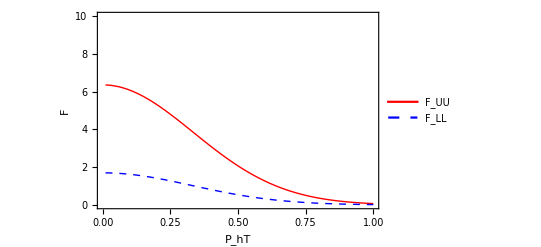

```mathematica
x=0.1;
z=0.3;
Q2=2.;

Plot[{FUUnnpss["pi+",x,z,Q2,PhT],FLLnnpss["pi+",x,z,Q2,PhT]},{PhT,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,10}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"P_hT","F"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"F_UU","F_LL"},{0.7,0.7}]]

Clear[x,z,Q2];
```

## A_LL numerics:

```mathematica
ALLnnpss[pion_,x_,z_,Q2_,PT_] := FLLnnpss[pion,x,z,Q2,PT]/FUUnnpss[pion,x,z,Q2,PT]  ;
```

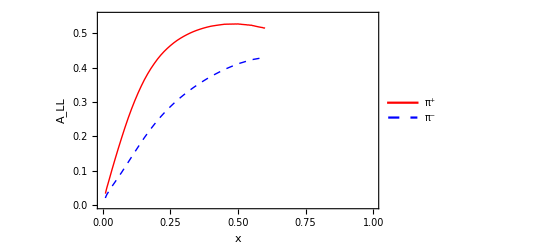

```mathematica
Plot[{ALLnnpss["pi+",x,0.34,2.4, 0.5],ALLnnpss["pi-",x,0.34,2.4, 0.5]},{x,0.01,0.6},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0.,0.55}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"x","A_LL"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.8,0.15}]]
```

Phenomenology of leading twist single spin asymmetry A_UT^sin[Φ_h-Φ_S]Sivers Asymmetry

## F_UT^sin[Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(2.18 d) (*Cell[GraphicsData["PDF", "\<\
9E14ARda;S<:9LCUl^G[Yo>Pd<C62S@P<21_HVX:?3`P;daUKVMdJ20e830PDR0_
AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06MWD^c;CMeanOkDfb81o]F
:S_mOP`Hf0A`YIbZ^7aL6N0<S;4319_H@>b4hS_bKC;=KdUJJZUkMJ]kU`LnmmjS
U[@NooFDm>gmho^gmh[on[Uo=^=`Wk[j>Lggkkjlom_mVo/7KoNjN/kEG;]OdYnW
m]Vfdgg/Q^OHS_Ng[noon?HomJfn_geeonGmlOe_g]goXGYfmlNGgkfkEln67mkM
oognm/ogWkg]OK>^^fOG3o[AVomXNgLOOOcXgOg]MdNSVoiI]G6d;/V=_[6TgnZ:
o/P?KEdofo_SLoMS8l_ko]fmVEQUo;GoL;o?_k2EIW`>mlNO`/3Ym_SZcniOfMlg
n/<Go;?KJ?c27o@;lS/b8knn42Klf^gaQImI:=KFSOaBo48b<2kWbcQS9:e/PjU_
Sml_4ogJoId`h;ohZITL;n;@n:l9<I;UgPZLJ__a>CNmLR[@^P^Ln/n4DocNF7WA
2Cnf@oO/jiZagG<N0Y<7PlWE/jZZi_kfQBV0kLS`^DfFL1<93=oio1]fR;QD<WaO
hUY4OQ[F<]=i<Gkljn4n^ZYmSWdGmQ58/=k7KDMm>_AXJ^MTmDioo>XAeRLljmYN
V?HFE>TV6R@BLWm<kXMJa5Hhk_D/2<7m4GVKRI7kYB14]lOOg3368kC81Sml7gmK
A:8BkN3O4SWXhBCXh932ocPdcjV;610h>@H>==fHT4mQ@dK[c`XQ;G3C]Q]mCIOQ
m4Z19:YNe;Sh=oX[SU9]OALm_GWjA=6?Xn:64l4?a7AJ`KX2A8CYKnko>Hk]DbGK
eT8EN?Of^m^nB=KMm4@/kl<llolYT:D9E?ei@]?ZFEO3M4?0]dYFmlP>BSK<hg>/
i_2E:GcUddoMI`[:DHo]/hX;2NbM`bMnTRa46IXb]ikjImn/MU73O0c4kO7Cd^Ri
OZ8Lf8=A:H3LWk<3CEDmQfWBZ@n/b9I/CCDnYo4nX]Zc@8ncJWfHn2o_K]406D>1
k[X23[:a]EZ_:]Va=GS`i]@?3V_FROnJS;EXgC@Xh[;SC6@`ELUXHfKAoVKfPS90
HFo8MMWe<_QVC]dfP?RJclZZOeY66c;Jh6L8PS/I7NZ`jDRaI>X86JV4=Md<oX;M
QYCL7Sm>YPH0SRa9=dk?DBR@:U``9;nl?Cik=8;6P4TmOOkI^h299MgYVA=@6hKi
f@14WZa=<2bi5[>f@LcDUSTeI[H2HHMQO?JMbZ?Gh]_SXhoL7T/[2EZL;BCChR<`
2UZL3@iJO3nYaL?D?HNjEOJZK9CL^JS6fMaN;VnI<kRUFe3SPJf?KKmAhlF?=8H6
=@iSMMFZ3nODf9[hmSR]a]V>UEjHKTFOVk5/e;RJdD>AU;TkD6=KUe3SZNUDG<>^
MNZb6ToXXCWekG56SHLJ6OMRXR_G^A<m5T=Nd^=JH32SWb[b?E?TGn4FX=6WeKTN
@4WXdlk?JU3bjQYoWQP6]dCdgECW1W^6acSPnDjeORD2gQmonleW3oNYA:Fg[:iK
O?U^laEe_Q>m^VfMTkY[Wn0MBn3oEKB]JVU`=EG8;3PBehAeQoF_MN?_S`Ogn>]4
0Z_=nfGW2Vd/^inO<i[/USe6b^Vb?eUV=WBS7RB^1H]]/X/<a4ekWfZ?OBeHSZ70
;alDcj9;mNJnTW3><YOZDVER=0N[L=JUbPKWH7`4iLjU6^12ef5^_9UG2Dj4a/H7
mJWlg87c2X[Yj:fl:QQWe5O>WO>YMSRG@X/a;cX[:HYLFWGR58b=/OR1CTdLZiEJ
^]og4gfg^1cm/HaCB^]S7L<GNmI8n=2bPVILjeRjIG?ZESaG`=RHn_Kh<95dHm=P
`X@;:4[F3hX=jhQFTSOFF?a0]fb8?UaOM/nb2BjghWTSWi@iLmJ^^e5L=jaO]^/D
nEeZi_IX=>`ESli5a12D7d9<kGkh8QZ5Pb1=kD4eTB[CkBZ7=niMbAkP`@iMC::e
0@nl?A1/BU1UBoYX3o:_W0AF]@Lef=JYWeZ[URBbJP6[fX=/IQFHa78K0U>[>O1S
ELh=:gHo<0N/^ZdRhObZKho475PcZcW8EQf]L6X>2?PUa2jHPhY@Nm3laJhm<<<W
]@MNS0;>I<ki@O9:@na<1W=kL3CJf`=LTXKP9k<7^CFf5:hV[C3dH6^fl5YIWaP4
Lm]R4VI1VVbh`V/bfV1ODoO?VUQXb0A71OH_a`QGPa?SZ6=eegkRg5GMjUWC]<@a
;3ZC6ifhH4lH<oJbHBL[:^fjh`nBEE_TKUX4LD<_3cO50;lMWX=0:k[BhGmiCQ^L
/VR=nN_9P``Ek^mjdJTY<ZP558mThmg@<:WZaU_9OU9DJ06SG3`DG@_A28V_EY`m
A:cAk79DkWC=9Z47DQ8=XcMZ/K53Ih>AC<BmBI9ZA9YET8C]YF04OgIZkkgT;M@?
ENY/K8m;X6oiDb?=4gCY2K_8<0CmEm?caAonB2Qbd_CdZhmL/C`cHlTbKUgj<iIW
=K7:m3W3hcN^@Wg=k/RJUoS]V]UI4CcT5UMFib0UA:j_8BgLS`P1JF;?>=F/SmIA
R0Vo`NYhn@UO^6Qd<]VkJ7?8Cca[P?BbcIWabHLPmV6d8VQR<`a7Y@6oa5aU]5OT
;YT<2SFhU[Vhj;@YWVaec9VZQQFW>ZKCoSD1@F>X82j5ZIc=4LN:1Z>Y7NQWK5:8
B3995^ICjfc6f^UUdfZX[K[eXn=E=`>9J1Hm^>BWPTZ@l@:aZ9M@0=K1@C5E/;eL
kc_T3N7BB1HYTfTeT0F;8BE/X6@TedXfnV3AY/GX:N/:63^QSTIBJIeRTCEL8iM/
gJVE23GU<h7;UfL25n;3FYJ;jmh?^UaMkFWS@NIn5>=1f4JiA4WVhaJ<6nI3C1ZN
UTAL[XIh7<;ddi<Z`?8mElXmRLV397VAeikBNDc=9A7<D[@im>HkoUE`]L>mY170
kdW5caO<K/TV;6HZ[W[JQTmL1MJ<<ENA5E[<Y0H3@eCn4g0lc>h4X@S35N>BdBJd
^XYICcSG8Q5nI/Fh4[CjRUTHZjIHidEbHU[>0<R@gK4VcU?];R>k4l=9829iWYc[
4FKOol31GH7]?]f39i?aGGGZf97AM8mXDSFX:ReXNdR2T2ZBaM?4/:IO2[NF]3KT
TB]De5Yf>EG4F:Md;bbk6g6N0=`GU`eFe6@`nhf/GgKA9eAND2cSF`ZnBn7_:o1/
94/D8KHP4gF;Sd?1X:mM=Co`AVERPk=k2J:^`FoQ:cS[e9EE[h>G3]2B8WX=J><7
Gd5Jih:Z[;j0]1Qjd^Pm<K4T0EI8jhZJIi7FDcMlhR[BIZbiR[CHdA7UNAEY/hD[
hYe3FT9CDInGT=J?GB?5BJ@e9Wh1JC>^_hZd6OUDZdhR;M:[nJj;>4_VJIQY^=U]
TK3LJ@A52Vfm7ia9>bGla<KI63doQ`6/=3OlhC;J//cdAm2IdEoO;gPhh_V79Ao]
ee`c]CZY^_LK5KT<d2@hl>SbcM_h;8e]10oWlIU^c7VnMi=d_bQ;EI1>`g=CBHmC
=d_a@Ue6>Qg0=8XF;WgOWTnR[3ic;H_BcLfcad05fE@7k5PUG:/In9g?[4ZAQRiK
od_cmf6/2/U9WcfDLfGEe6cbEIo;ggN[EDLTFFEBjTXhHeKSB@IGm;MeA>MSK9V8
7_nEC4X@Xk2?RgHXUl6[MXR6/FQ3@h]L>Gf__CGi^RnI8F7Mf:[0ZKbMLoS3F9DI
WMO[RXoa]`;G18OOVSPg@bHXPH8CCNgiSUGQSmE4OOAlIUFCa6QKl1mlm4hJZM[3
7SMSbl5fQ<4[fe5<RA3AEZR5_NFbkIP9AekJ<WJWVV[V;FkIi=C0/RO/URWI:BSI
XgeQb]hdEEl=:Llf4nDOl/I73SRTnO_OG6/VLWg?R28QWiSI0=TnBDJohO_^^06Y
TcmQde[Y8/JFl:=[bHjMc[mbOh?5ffl0_nGW2=86l;/dP9?Hm?gO9?cfn[mI0;mf
LjLSF5;/ZdISO?glLkMJ?_COkPLn57n7mK^2N_aMoblLDhSKdEoi;_aZg5i/dXio
XklB?omjJgNiZCeb9f3Dd[hm;b9TiU9ZH6XFZe;CR1O;6P2=LghfW/E^MHHj8CiD
if1;HjAPhcPa8_Ve<gd1U8SGglP/M>PG<R[/m0Dd=F@PTMbA7Mgg:n2af=RM=WCR
C9;W7Dio[9M42g^^2IfdGTlGCj1Wh<MY4c^@ARM`kXQMIP9Y_`dofWF3:1cH_1c9
XU<fb4N[dOPGU@@DZae^gg>::QbA^]MaFYBFV^/GGk]S4eoO4HZV6OW3knnOL>iZ
ig18?N9GdTX^QdBZ>FaIYoeHYmdK?0f^?C0G`>1FW>VlmifPWCAfmi7a>W]RkLcB
TRCD98nEcjhF?QU]fDZTY:4FfB4dKM>5OIme;FR:9:lMaZZlnXW;UGelVIY5nhW3
H9fhE=TW1Mk;QQ7aEYTE_E70o534T0JhQIi]b>g`h^nBhBj?2D?/he2=71JRTB<W
_6NKe9]o41B^hH`dPIDclXd4LL@C0T3>PgHaka12V`8ObM1=dn18<Rdi4QD2cD_^
7HeZY7eGo8L<@EGSdbICd`6@Y5hT`dYg/26A6hJkQL=Bhd<;:lMhlTKQ2R<OaiXC
B`68HUnnK=DKlXMa]34cA`ljYcDPLJ_]I568U69kN44;56Uo:8H`SK6`ZRSgOlWD
e/9KNU;T`96=LTW]c<Pad0f<3l?@jCU3>@n_6lmh0LIU;PN<]`DH0BgHEP36U_E?
56Ll<8KYPX`oo[NdCk@K;=iZVX_Fge]6Vl3FRRm>9RIW[mGaI9ZBU^iGCRcZl22G
ZQ;7n]ABH^b1HQ^NSS]XFmYQ11DbI3<5Jb^E[GSRi;33h1DN7l>R[;TVMa=PLHg7
7bcD]/W56E4ifk?3[0@FJM6SFF8G5]/AJ7MH]7;77==ol6XIL_T2B0HEG1S3DW8T
33G]U7>VLTV6XhUP]/:SA;V<VNWF`_e0^dPMPPY[6YI@PJcSLn;XGbja1XjJlXhf
^X9j?U[Qk1Q81DT2kl7A/>L5AaLT]2SFXFR3B7/6oj[TF;437>eX>R>CDfKEU/dj
5433IXDeVhYR;QYa[nQ=N@f1>a:^SMSJe4UEDV>^oHhG58fo_`9A=PoQ2QSJLC8=
[akjRW=iP:5>/EaQb]ja]5;^:NQk?ehGCTndbffl5hff/c=hloTcN4S@A:FTAH>W
f?VhN`K?KGD[6=Qd=S[LFoYUjdR`81V4/U:1Pd59?M3h1ZGFN^[FgkPBRTe/0heL
RX3ZWZHJhEQ68MQ<Mb9M064k=M:P7oR^B_WAQEQ/E8869E54nHT:jUiP4X:RUWAi
SGogBRc6g=UXEI8HRgf;QnX>RLHH[2G5gg?0MG4e;/EP;CF8]UH@doW>1V6ij5d?
`[00dZdCXVnM?C4j9WI[49K?O/kIJ0102L94g?]N4iHZK:Gl[Po2`UQMm[DP;1n/
4amk6`fmcA:41N5NXoOk1LV<@MR6g4H@APbejfeX49HCg[?=1F4T[fSd?AN1hGga
7APQ::lW][a_WFOh]gPSdE]71==:WbZ9Q20o:P69if3;3a7HA2]L_PgElc<Af0A>
QM616BZkaii30eB?^9bbl8[kAOc25JG>Q60SiJAlgC[cL@SFL/:=<Ve;<HScPV/9
BRQVnj_hF]979?N9c;6PMCh2XenBHb`f]_eRTMjM2:agHR9M=H5PQa5HV<_3HQ:1
DMbVG5c`7^@FVhYO2k0HiP/BOR84`c6D;<e6dDk6H0CX>1diOlo:ID^OIlDYZe`^
EBLBC3ELlIIL?GERALF`K@FWDPQ6RXOc@CV`VJkUEY=K3RA8Ij@=alNXf98jWAbi
DY<O?IMb34I<S^7LHMJE64b^MMYCbaml>g8Q1R>=BoG>`/9kMQN0iJZ:FTW/WC=N
HJ4DPm5EBWPIL24`?]:`Q0]M=D^K[DhMQQ/BJn9`Agm1Ab]f;^njl6<TkKP=Rhdc
eR5Y0;@5BIL`bR9IAo]J9hRD^lh^j;g9QEQ7@AQeah6TOiUIFg7_M:`gG5MQF4YZ
dXGj6Pa;I3AbcIT=`coCCBl^IQb`MS5YFj62FH3B3_DT?J=@^[:CJCJ[48WQ:0`L
DUcde?GdZIP@RZgRTa>QV5bST:^;aV9IiG>F:^BUTd/Q8Z=K^6XdFJh[gAC7BQ4I
GTk;4C?eKYJnVoF>]h8VQfIMA9IoHhW8UVC_GW4<2/T]J?5bUj@ALU6?hn:HSlP@
>jkN2m]@3Ogdg>D^[SZ6WVH4EG`i7I5QI42Z39g>E/NH>a^]c3b:b7XiL36l795Q
ao]>fiee_]<AVJND2/gi2jUlFJc5=IIk]Ej=b;;IcoTN<B9c9AUEV/GgF8A]:nH=
OH=B5V_mF5gfaHP/6j`C7o/N<B;c`[d6l[<AfIKLATAfU?n=4EU6N2ld=eLD:nE^
G30/D:g>]FYXd[]YF^n6:A/9BXfYG@ahH4<Kl]l=H]IBBZ>?<Y1_hmJK2N^6a_RF
f4UBl6g/d3[]/W3fbmemURmK8BD9o^a=TejJg<8M`PN1DbDmMUVJRO8EMfK9`Y]N
=jgTCYd>bfEYIU15g7^3g;O7lITgJ_BTCQT:VjlO0I>ZE4/=Ebjf93/@V:DD:iOO
i00=a/B0dM/S2Oj//8AVTdiL2:hdJ?M_k5Pbae8YM9=i2;hNoM4D81cb49aamgHZ
nY<ShE^U?Qom@NF<_d[UA2k]05f2?aYn`nS0Xg<0k88o4YHiR2X>UX<onZQGHh<b
LZ>L>YFV9X]8S29H9_8O0k0;oVAXjUc4NOfiY_gSU2fifPhGMXMEBNa7nhoP[nBL
;JfDFeYk:/<iea@?l_ZKOK=<2bXd4T:m08D]_C2E^;8I52ZRO5BXj;MDm=/MA;To
BW6Sa9a2O`LYJo^Gl]dRVmC^Y2<U9i]DVigmBi<EiW2:M`>m2?U`YKZR/5g_U2XD
9j8LcD3QX>=:/a8:BoG>1KaNBl>nMNIdm=IITA;Li>S]S5jHNC5jRd]n==H`NRDm
hcHeeg8Ja2@/F[NLf7UCa3^f:TU7SoiQeAjGKXlBnWM8IXm[HJ5ohRBT<FLH/7JR
CaKoY>LD>39mj2/a9fE]:FQ5MkP@LiYB6Vi]bZEd^D=LKZ1`3JB=JcJU]GAkJa?]
V8Bco=?IFi]Vd^4]YG`l/iE`K/;?@VmVBkM=_a`heV<O5gXcIBGI=bj6We@VJmXC
@bbR1RUE/^>28;fIm=a@gJ:YIZgX9blGeOPcXjPJiM?a9dgbg7NfDQfh7SeTBgaZ
eid9AVJS5FZ>hTnY/b>l[eH4YNMYe?I4WNmdo>TYYDbk77mbcd5bHTIWC`b2jIIc
/_gIRcg?Ien`mISD/J2H/OVLmaC3EkVQ==kEYL9jk3g5l3DK6kfHe8Y^CH8LbgHf
e0l>fZhC7g]?<Gc=M2?6D:O3Ei]KRO]DJ5n:hF_6=nGj3i@CUo3E=^L=B2nWVeXi
ZaI3Q;>f3@N0:l1aOC?6jo`O9QYZd9lhE6hfKX6Y<IiAFTC^b9cSl=6::MPTnG=E
5QFhU>lF<S@dOG6jN;GZdkejg:e4hH<Xab3jkJ7NTnf]=ZB2FnTiHN5MK79@LZO@
K2jLJmE`mWGVUH4ZaK1/F/Y<<5XjcS@[6W;f9IZi`YhDRfQ4UVi@?ebA?75SC7aY
YOhYZG<CRhmMiEKJM2AO8JkSoX<@JA2[TjeaO=e4JZnEIX5IJ/`Nal=>EJIC7lQR
TDPcM`:bFPO4PDGQi=gmlEjR4^I`KV=3X7?A2Y:IEoG=dEbMd0eA?/;BEBeB8k1E
Ao6b1ZO:=Ph_5/0J:agM/2R3dY<hg883CYLc4?LhW1oL/bHV3`Ji;1Rn?lXEC2B;
0kXk_4YP>4BaNlge;IM]CIWi57MGABJ_H=Zh857/:76`0HHig`dR<9HlGXJ5RRRU
h4ARf76>0[M2U6?5U0M>Y=_jADBA1T=a/g9IEdA94SJVU/[1XlWI;NN[[kCd68@k
R3a9d/F3L=RdTZ`4`_;/RZC<COA?1flieG5OAbdC6ec>jm@7Hig9DeaAgDkQfaX[
5bJ^c:G^]iCVh<DUWbl^8Om>m8^@L4ET@?jEP2e5Dlb@kl^C6ZdO/4;_MM7D5P^i
gY5kdL[PGBZJdVD/nITM67niJ9XiBWKAm=OGRjI]emhK6/4hDk^Rl2IZgBfJ8]DL
eN3>@011SfZTUaFT_Z@=H_CN^<;fjQ]WXeIaa`LF8=dP6Vk6X^TWRN4/5De91O9X
4@O=<6ONCe5Iom@ORTjJLBdcFXNX=JNX8]?IZ;G1FI/h4I9jB^N[Y_UX=BD7DF]3
5d^31GTaJQFWU]NdE];cLD9eTe;Q<66PE=S[iCiF>OHcaJKSj2bU3X/e^hJMnN`:
RLUXXcBRHJN8fcbmESD=HgGGO^;KXo0620PPHFLnf0XkcBgS@3M@:U1<cH3:agVG
ABi4U7]25mYU;X]_QTcdI6]D:7aja22T4ALReKCK`b_JOPFQT@NX:6/]ll/3IkZ?
a?4`NQZUnXUZBb`Ukh_iRDe_db@Q9HN1mHJIUHA;h;Uh^^I`FYjhYUV7QmWm`X_A
7a3MLkkGEC9S@hF2DnXkF3=;2jXl3i8_G4VFS]hbB`Yk5EUXTfKinEMcJV:`PA>4
/XB1XbPYY]gC9;IYU9da9Sb`<Ne3aIPTPY?@b`e`V;JD8DlU/E/iH/mAQP1Y:`jE
0cQYdLE7/c4Y2N3<_MHLeJa83SBBOeM2WDl]B5f7gVRAL6Xl@CK?8YX48E2Idn5;
fUN1YI188bTP<EPn=ZYDVV[MbQH?gi2E@2kma67A>W4YT@H<h<Hg=:W9na2I;]nF
26jASDI9A=6cXaXDkAeKX;noe5DWelC8<FMi7@`<38]Efii^e=83^FQMcQi;1ZV>
3l05PgEkG85O>CKBi6:RZ/aIK4Un7J<_QM^9Z4m`E6iJC=6G=b5EYcih<jFDjXIL
BV1?7aGB;3YSODP0@@::cg0n4=12Cd=B:1_gPYf^nQMm?3FLJA1SDYmkPi7AE;>D
LDVhJ8HQP[Qbf=4?3X]FNQm7RhfkbHP=4iP/UjL^X;gT:LdeP`Nc@7jjJYfhU;6C
9a9OXkBP5nY[4U[:WL^R]eaZJDZVF[TJ[1]>A<^TM2/gP^2oLc^eW;UI:ERB:;A7
TlVIdF81@1EZYMH_SUO]BVD<97e5R]C[`dH/5abAW96KbN?8HV?T8[hC1ad0_HYl
J<2AZdJ6mU:fV4^5IBD:nGn2NUh3FUTKYIMLjK30R9gnUk[b@4]Cd>Hm/YU84<Mj
K@jL?RdW<6XD1g2[6:GKINE`RM`]m]:R^LIkhW[HX1UQdM7BUB18CP_:>cSIZSd8
gAhU46[10P;JK:`bjaR3^PYY`id86;@RMN[jFAQ4@b[B]T=ZknW_gJXVYja7/Uf_
T;[3e0h>LjGGCo_eC59_@DS>=TbBeLQ<QAN^LW@QKBHEakD220FaEV>AP91Y7C^/
O4M5bP:Q938aXTYYDI5H::1@h=<12/FYe]j<M>iU5ek/[1BOSfZ<QD;g[>6^T>hR
UY>kWX=OXeZQ`[Tm8f2:FNSGb>CkaGJ=DgOE2he``/CoW3^e=;[VCN9[]ef3d@8V
h][A:jTNJ3P]L;9M8bBnlVmLC7aAoiR1Qk00mIoca9Llo;5gOY^ZY>@E/;lmBYHk
Q9^7?dc[6a=O6DEEKDhW_RAAS<_SEj3PF7:]]EfSbDH[=hlBGaQn>G<K0`4Pjl8U
FPfoc[/0@NAe_]>9;dlYIM[EMXf6ldaTaWFhcYjT[TbeegJ=8?TjO8<cV6e;DF?N
;6?cfBSCWonFBbliXABVEV4]A9VhG7;J81lK3L;9_9VO>?1;9djSC7?;8FmV4_aJ
h1KbIQWSUG6Dn/ZAVk/n6A_1WC/La0hD==`VToDBkm4?V7=NYclfCV;>^>o6CD`i
Gd5NnEibOJCaGbi:b:MFmBki?Pf=oaggm>FSMN69mf?UnjC02JFTH`NHF56/i?e8
hklLk``c[a@m7Kge@]Y:;]RGVNGPX<hL9?I<fXck6O0SZ1QFI6IB@3bA=B?AdO=j
RPf8A^E<VRcL00n8BdBc[YbIX22W56[9ZWXl38_e33[A^bnZ;@6=3FQW/fJeG:92
n9MCZRQK8BDT/3R=:]PZe`VH6QjK_<7T/VIhf4]KS<9:0LldJiJ=SGRFF[b]J8Th
^ZbI7gb0IlIH5ReI/iYRGALK8j=Ha[j79M[E[5U=UHSTCKBEei9Vg3E2]:S54_D;
dWfJf:]9<mj/BQYREKB^9leb:E4<XM_]1?Kja_NJ^g:4P;VCU:@fM[2GHnKTf^ci
?eabKYJLT@jAfeJ5IL>TcZYU/@efbh^T74kQe:eDN<>Z8k_;`<fDCUYBiC:c3BKk
Z?4=i:C]GBO8KNeJKXVQMl^]G3aGMdfTf[XDNlfIdNNA19PeLoW85^XUNoCd3S@k
AnnFaQKY00_d?S:DFfH92T_j?FOFfL1ENVUJ:Am`hXbP9<O1D]`ZWG;bj8Qc3dUQ
nM6Z7lO>PGBJbj=k3AJ?Y6?HlhIN2j8/TnF8LRi`IHmDZb6B0iCEBX/U6VZGTn>]
4nR`EXFSe5[h`dNkKE_RRHUdAZ^CeD2ckUVkhl5MPDQIcI:bH]^FG9lXHc>]E]e8
/<PfejCQi@6Q/?I00nGe<AKaa:fk]=EJ]K@Q7BJ7bL7Gm8OTZhhf[hA5L^9:O9Al
fAK[;41XJJWXB:l/35^:aZGJ:iT2h^>PUo6n92Eg2H[TXPhNm]FIEn@^iM0P6Hkc
:nBFnc7Ud[hCi=i2TMcAR:GC`F7A^^FBQ7EL;Mm8PWH;ABO>;I7<V>SV]j4X>KEZ
^?]h=>iVZ`15Nm2m@95L;n/W4bQJo=icVGc95DjPYHE5^N=KbZ59hH1LW>GVd?Uk
nL[3l?aH;^aP9ZMQEbl4c`SPYNO70;a>38FD0F]eAQ@l=YTcISA_39@[/HC7d/2k
M>oX@BOg_Xgg3@l[VCEFBa9`ZlnPJk;Ak?HNhjX=@/:IOSmN_dh>4LB^/DB]3D6[
/GWBJYS?[3K?]oS]9LKU0CM^G=Ba@KL48MaQiCCX<5I=VUQ>4<RZYH?F6nZ`j^;k
=Ya6U?<BnJXS0Ymng`KWR^LkT06DQZA<kYY]6^E<QeScQD6>`SLDcLoV2kT7V:Bi
BZ6>;TDEVRl<Xl?LGXI_SbEO61];mM;m6[]Kl`QVS86@_`_i`YZBfmbnVRo<:GFi
DJjFjhZ918;0n=eVWL<VWbCjTc?Bg5cW3ROhhNL3I0k0lS@11IUNGGP/TY?cdXF?
F4e<B1R[boHCikf@Fn/U>ANi=3`O[1>W2Cn7bc/_C4QlGi6W55DKUXHLgC/_N2He
d^B9QXETCUXFXg8fHYJ;2X4B;bfII^@K]o`LPTcBCT8gTme9a5bX3cL0cB0XiH4n
Da9oignY@=c@2m]@a:_9>hhaDggFQfSTZWn19]?@77^YDT<KZEX:inIhH4WAnMQ;
UBJERChMNHE/boBBTh[GPnNc=Xl:C6UlHC:?g49=niU5li:C:TfQ_9KReRgmMSTX
9mK<SPW4Dn?l/Tg]D[<9kA[dPki2KJhOYJg7[oZHfU/]UkCSb4hmYbjjZ7860m>5
ln4^`?ODlW`Z^jP^e2JgJaV@NgZaR^4ib46WVOjYFV@d7T1LI3>dT7hKSLlbf@Y>
c_VXg=N3X`IW<cSal9okZ9I4]X82S/K>gL_0j9if;AC@a5dF0P2o32Ibe</iS;I6
;hfgQYb4XDjQ[hZ9Jdbd5ek/=A4_G?1_1hD>eda172^FbgIde4XX9?Mi3a:`I^BF
]<Ni>ck`cZGG>1o^ANHNCjWJGD7LJ>UNWA6U_0i3GDgAQ3>^=PbEHVG0DoC:UY2S
c8BdZTSKKaWc]m8U;`;@e_`B2<UMV=b5b9YO@B69/ROZHSH:9CTk0hFjS_`GgEnW
DFRIK8e2jfhCdki8H4j7b8/Xa3=6[S5`ajTYUHPT3C69C`@DRWBUH9n1V;Wd1UbD
@e9QM00@o[b9e[K28AFaGU9]/6XinPc3P`Ml99CBSC6:TLW6APa8PaaSH[Hjdi`G
1XM5jlBY1fb<IM4eEg7E8]WKb^E?Tf:5IC:T6lJUAQ6a:_Iba9<iEca@Kb5c]RT<
iALlfF3Db1Dh9>aZUXCm2hcWcfMHAiLdCb@j:/bMm]<SA6i/:@<VgZ_`;Y<h_oAK
hGhWLD3UX0@YFW8T^^S8m`CkkH2=<bXSa`ocZ@DH=i/f^BMWE;SG:YMf9GZYI<<A
3c5hhU]aUWc]PRkBK/i<Rn<P^V;@k5jh65QjUVNIfC<jR;^eijfhak6/6TJ7E@Mj
ihEjHc0kZAdhY8??BXVhMQ:CeeCiJID<bnK?SUE9cLH49RVSc3:gM2aBRo3TER6;
4E;RBNX0G53YiXQYS7=WHeR/93mZj_Ge/3k^UaINSY>MLYbg4VR:n52hh>W4YL9b
Kdd^/BR^435oCWDVT=Umbe_DGLhWfKO=bO<1D^c7^iPJgO`bbMnh;H[KRWWj=7/0
kn?o1j=D7ad:IFiTLgAbIF5]2VE^I6mRJPXe830PKf9Z2STb>C0:IFiTKf9Z2S8P
<21_HVX:?3`P;eAiL6DP;e1QIfDP;e1QLVE^M20c830PDR0_DVEcKgEbHfEc83HP
<21B82m3KfidIFidLb0d830PDR0_CFETJF52KgPPFc0P<20e>CD^<SLf83Pd<Bhh
>Ed:;d=bKg12KgPPFc4`<Bhh=30g83Di=Bhd=C4c83Da=2hh=S@c83Hc<Rh`=CDc
GB0_@VaUIFA2KgPPFc0P<20e>CD^<SLf83Pd<Bhh>Ed:;eAbJFe2KgPPFc0P<20e
>CD^<SLf83Pd<Bhh>EdP;d5bM49_N21K<20`83Di=Bhb=cHP>3@a;SPiGB0_DVmd
HGAU830P?Sh:IFiTKf9Z2SHP<21_HVX:?3`P;e1bKf=CIG@PFb0_D4A682mDIGQd
85dP;dI_KW@P?3`P;eAi>20a=20`858P;eAi<C@P<S0P<21B82mDNCTP<CDP<21B
82mDNC4:=b0`858P;eAi<R0h830PDR0_E7Tc83TP<21B82mDNC@P<C0P<21B82mD
NC4`834f830PDR0_E7Ta=R0b<R0`858P;eAi<C8P<CPP<21B2RmDNC4e838a830P
DR0_E7Ta<b0a>B0`858P;eAi=b0a<b0`858P;eAi=B0a<B0`858P;eAi=R0a<R0`
858P?ShP?Sh:IFiTKf9Z2S<P<21_HVX:?3`P;eAiL6DP;e1QIfEc82m=IFAYHD9_
N21K<20`83Ha<R0g>C9M82m3KgE^M20a82m;JFAc85/P<R0`858PGB0n?PYUKVA_
HVX:<S<P<21_HVX:?3`P;eAiL6DP;d=QM65/KfLP;e1QIfEc83<P<21B83hn2VE^
I6mRJPXa=20`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9Q
LfE6Kfid82m@CTe9D4<[@de=BCPP;dI_KWA4IG=SLVU`M6mb838d830PDPX_AFiS
KfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQLR0g=R0_C65cM4=XHG8P
<C0d82mGJFAdJ7<PFb0g<S8P<20`2S0P<20`830P<20f<CPP=c4h830P<20`830P
<20`830P<20`830P<20`830P<20`830P<20`83Ha<R1M83hn2VE^I6mRJPXb=20`
86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m@CTe9D4<[
@de=BCPP;dI/HFMc83<b82m6Kfid@T9_N21K;CDe82db>34P<C4d<B0g>35M2Rm9
M65/JF=1KVM/IB0]<C@P;d5cHfE^M20g=C0P;dAULf=UKW@P;C8e<20_@f5`B6EY
IfQd82dc<S@b=B0_DgAUKEHP=cPP;eQ8IFUWJ7@:;C<b=C@a82mCM6E]B20c<R0_
CF5hEfUTM6PP<C4i=R0_AVm^M4IYK6DP<SDP<21B83hn2VE^I6mRJPXb=B0`86mR
JPXl?20_C6E^IgAX838f830PDR0_C6E^IgAX<B0b=b0`858P;daUKVMdJ38P<SPP
<21B82m<IFiWM6Pc838i830PDR0_AVU/M6Eb2Rm6K65dIDAUHfmTIB0n?PYcM79U
HFd:N06<^PE@G=^f=XZk4ecB^;]KL7MgYg5gM`_^k^h@84Q`P[]KL9L@g>fA_LoM
fNNnmn[oZj^jecO6V=lL>UMe[bHSDU2V4cBa<`::fMTjdc7A<g83Q6EU9CT1S8`/
m8b<c71TI2XFc]K0ohSQb=B0SThFM[KLoc8@MP@J>[o;A0bMgneTkF`1DRkF02HF
01<k=a<7=b<SP9VATN^MjBm3>dM^P8RQZhD9@9HN86EW2gB28a>f/oM`]30cMgkO
iWl^0IC6E00V;Rh>f[nF0`A]P8hFaXJf05U3Ig>PcO^>aXKF06DkH`^P/lMoDE3b
VS/kfg<c<;Ri^M4KfSSAfcVJOJ:R1KQI>9/3U81>@4MGX0WPMl00>D<Kh=l1dl>A
0EC<;IcnUR_KVCZk6CX20Nl2J`]SX:gCn`XGFa>P8n1mLh2bY0a0gQiXnkNac=l6
]83oi0K0A<od3meoE_lV/[3mJk6Q/K6MSKfQ[HN5[AW0e<8J290GTj5gMWNV1ASJ
V_`f=;Af/W]gam3Ed<;Jd>SMh2o?3@5RPXX0`oLLoBLl9f=72g]W9gXW2n_O8C;l
YWW?/ZR]RK2MS@g@e]T9kWN@8QJ>@6=W>dL?Q[l[JfE[ifK[mAmPJV5[H_Xk4bH^
mPbZ]QH>;T194L3O9^lR^3lb<j0cP8fATh>5T`D0M000gHg=6GkCZgSH0`6oUDbo
aNlAn7SIfmT3C=n30?YHV0;O?n2lW0aMP@1WAaNPSmNo5On=h9RH02HFa/h08j2I
QBgL7oIg<M3dKoaNO4L;Mh0fhg]c<P4HOkon^M9mkd<C>e][ScoVOmFG@DU>DE59
S^K_l?nQ4Q:bL`MhdC6c0^RHfAP1C4a<S02>m`^OojIA<;ChCi2<OgPUKDg]0>of
OkWkWZOoLMWeknT0D?iWO:P0oddVIoON]T00iIl^ef5THcAnOf?j_nie`>lUoel]
oY_UomCUom/Q<AM[jknBA?UGM_iOJT<K2f^?oaRlMjf;lo/4b=Zmch7]ocIE1ohN
H02U;=34`/GVOf/UW@gO9d7@e^bmVnVHF>TIFOm>YXFCV8Dkd4C1`]WHo>nNnE^^
nW_F[2e/P@YfCQJo3iOgENl7bEo5ndOg?Zo6E^l7R==kHoj]<WAjWeGW_l[hfaCh
?TooG@1AFf<kTmn3alc63S1dM3CdP7/_oC]R0gPa_DnX2M3m[mH6<=3KfSVoL`3N
HoH1V=Xi`_d^<c/KP47`]nQ_a0iP4?Z3>00<`Wl@9h11i1o4`@QP4?^3V04<4Wo@
>h_<7oC>8_/7_K?8oH<hgeTDoR0F08?b7l@:H53iPmkmE?f3gUTdoR0^08?V?hS[
WE?[3g[OgO0Om3j?38KFm^Io95c_C4Iom>ma606MojEnYcKnAlgf6kfOA7od_d_8
H?:?0M>kcbI0jglA<;d?=@?`Sl5k643kmo?=cYKYSi3aOM^oj_9G4IPHgo=PmTOk
6aWnmjK_fiSo<F1l9kGh5ga?_nFoh7/6[?h5g`>foQMl3lWV7lSlkXR=bco`m`72
H?/_n:jfo`Nb_C?I_mo2k?k4co9^KfonaaOVMlo/od2Vme/XPl<o14a<kfZWOb3k
NjJL[0fMoQDIdg/Xc_lH<36mQo9_kmhML?fSIGkOg?dOn7h:<[SoJf_VMgJ?OkA<
_b?eo0_nohbC/_?kbFoXJ?;?O?dN?f<GAlOgLOc[T7`OaOo1OmgcP41gX37LlX:M
<Dn`IGe`ngfM89hKgMh4;nAIf[d6<me4TAj<LkoXS?iFPW9feXYdQMQb7i>HWVFG
W933OLkjhYGGK/?7APoFFkZ?HXMV7hgR5]i^@NLB_Nk`RAN@Fd3beE>42;U;7O]1
50PRDKYQnDg<nYG9T;dYj[l_9KZAObPChi0:JIO[k:h[bi;1a>MBnkV]i=aZ=:Bb
agJ=CI6kKA<K]1>UlcUE;X=HV[Oc0Bk1[AIULg1TJ1FeSj0W<T3:=G3_W3CD6EFD
I`QOQ1FjEVfe0>Ti]mCe90?=bdPLGAQCFCJOB0TKKTRh8:We35_WV@AJ`c;[/gTR
g0TfLTM1aT6a^IeojP<;Ffl@If[^776HFHBG2NnJV99oIn]Rf<P<e]dbi>K8[SEl
me@KIAJ9]gUEfJFOkjRPLZAUFXfa5QfmNQi`0Cfo3hgJcIPAoZiEW2VEecfW_nPb
[C>4FmDLL<O9YoS4;Y=jjF50j8IO1QF;C8OW8VVeSb[XV]/CkA:]7;DeKQ6Jcji@
QPnSIQj9Sk4CMUf1A_QiH@N7VeadTF91T;8dS7>Uc:]F;R;N]amQ3_ZVV_03edLW
93j971<21bnSKH6?>fRJo[TPHbB>`<e4DISHnhnTe9jflgAEgm^F7>U@K4U:?/T]
QV@OOWH:YoPE@0jY`GWEAP22RWgmo0>/[_jFiE]nFVX;@eNG`AMQe3PFSV/eJn8A
oiFS^=/78lR:NB`iX0:1P7@K]9YaSU8`YhPi9eO5bM==@IjmidiNQ/aIYURfWnkl
KUYk^hdfW^KcKOkQ`gbSk_NT>l3EKHCnYKVJ`J8TdjWDkNk;n7952CE_Wgf^Ub_o
7H8>OY]hEj[^oM5AeRLA02b>lcRlJPW9jaWW>5H@KLg:4k2Sh52L3T2e`2ClaTYb
b;DmgbCTVeZAM2PB:FT4lgX3Y@o?CQ_3ak<JJDLk9GLS:I]U6JOok:YV1k97=XAZ
WUljY6P12VS=I=?PGAnXZ;9>I<b@`@/:kX<M_DGm]WjFl64KT]L`XOE9PC^clLU8
80O<QPB4hQi[if[EM;8a/YXH^7_3ATAeJH6=WX8[aIeec^96R[9>l5R<i1BF_;mo
O814iUgTOidcoCEm_X;/3C5C7XFhmZNKVU/mXeCjJkH>S?i:WFSk5UkC;m?;h05T
1ECH8i8AAFN7kVJGClJ<=:@Sa[WLYo>/96</BSCV_Z0NX2a/GfYN]UVIYH?;Vh8J
KfgfS]OD?NWa2/cfR2bS1B5`lkeW9eeS^5:1Z10>]j=[0aiRfPjmblP3_JUPeYHQ
L4NgNjDPREWkn;5DUS?Y9DkPWja;jo3:DYS[:l`>Y]<PkEGf^`API1Vl]=^<OTTc
bJWW_7@@h3gZ;CZSnh^D4PbCo[STfNZ;XZEm2JTnKQ;BE6ASBH?bjEKTj7AB0[B=
N[<B6?JeAShAeXKcLBjF<bGWJIh5=P8X;WV/5eQ82>bU?n=VPToSV]RQOhh5<1=h
mBP<l2n/FSf<_4AoAI5fjE<U0e_1:?=[Ha?@Wa@bC:<nPiccDTeXSld<@Z<KK5T3
4bl8[FCZTL7kc:KJ;LIhm3@Co>UHEPT;0G@ANHZ9b/@Qilj@UWLal:=BB_9<[e2Y
Y]nbOWimBUicjm`m4dn1F_V`>/HS]Ji6>OlC8_lM3368]5I;N50XR:F08RM5472m
cGUKXne[`64;kbXVd];3]i=TZgdD[m]Q9cX]/=al6`N74<LnBCBK]CT746L6;/?L
D;T?TE1VaUYWV7=RHJHe12;NeVG7<W6J3ce2UWMVeHlQMIVU?PJeih4kFGGVY5PI
nj@I/BXBoGAX5;cOcOC5=3biKGK_a^jN^TQR]K=a^9]mhOQdbTA_MfmV:hd6XB6A
XDnF:kKLL=HJHcb^lUo8Y]:9_4`[O0<XgG1EOF@7P]VOHM25?ZHcPZdDW9kd[mNA
5mR=b]H9<HZ2^85PEKU;a>QSTc7`=bmlScAVPaQf_iAj19lNUiaBNN7aCN8QAmEi
S:N4UHGbG;EBYP`7OFR9T2ZLI]9C]M`e>P@6/C<74]3DL_>gG27F3[6@_ngBWH]f
J5`bJ;No5;[fI7Xf2dQOM4JITQbg_OQ1GjoB>8W5lHci<9I9:nKFjV1g[AIXXFCQ
4Hd9najbT]giomQh@l7O54=iNa:_WTJANfHnaUF=24SP2YB<Va<jl2MPHklTfGVZ
FROAFVLS9jH8_EfYmD4=jC6[dShhl4D:f6YXfiH0Yo8iEIh=FSPmWL?cX2hHT07`
mRP?C`gQNe<In?MKRfmY;3d<kmKOGSKVd__d<7SQjQK5;EQSecC1HTfGXQ9STRZj
R/k<ZWGPK`iXiPZ<W_J27OSPdi1a?LbnZ:8bG^8<K:bobA[3O]o^J`_^H=9kZDEH
A9dcZLCGa?JV24Yl2:[TOKkFA<g554FA;n8EY2>5Z8nS65j;jT6Ael4/NnPDTQB6
f0gdZo=fRn;LJU3=W>g>^bYB4_PR@2nDje<6DAc5GQ0D4<PlDZPB;5oFohXGR==l
PJRkWj0V=bRhBbhi=lJ/a7Ce]0@O_K8VD=H=?BZDRd>ln5<h@Cl`2l//Kle5>6Q@
?D73G:8oXTZ6oWBKC<GHdAOOJDQK>4=BJ@bk>J9aQ691HlUTP[f68TG_lU<TF?a]
_=9V]h_JXS_9IMHW3i_8K`^Ii9]@=nkOX7;?8Y<Phk88[f4llT:]7YXjgnJ/g2EV
>5Sd8dnF?/moeF?<e`Z<DihTFd]IZNA;]HAbIm=@eaC9:SR49PZoJN6U37P0;YQo
IhonG?SE_3V_JE6XjDT06P<W;6nOFOihF0V3T^P8FoX3MMeZ;F7<BeY;T_?g4Kd3
j2FTRe=R7R96J[`A>2P@Io669kS>=bc[FThYCN@hkhBESg3O:]VT^B:3H`W>i]5F
;bi]/Z0eIl/7af`o0<B6kSkAlE<e4@nE@SEcZBD=@^7?DYM4^eTRcZ6?V]f?[RCS
Y4CIILW/mI1YnX9YbHjnm02h4H]c6^=JaQ3J1Pjj@@0QTnMg7OUA7g8>fhTDR3XW
[J>I6;g4NYb?:CB>Rg;Rf`jT`OY4IL4G>FNfmYa_5TK3:Im1LQEI?UYYUL73YXF_
IakW/mKWCUWXLf5>4Y9k58HkSEP;cXfT/U27Kh<9^5_A2X1i^gO_[S;T1Bm?chjT
;5;9;o0:Q_CRX6YLZlf[AD5`QhAJje[f/UX[FJ4m8[/7><CU5>TL_J1Hdb`6bN>e
?o:;9FUfPaVZSonB/0W:?/j_ek7>FH3Un6ALC_dT0Q@]9_B6=Gf^b`<EMdERAmN1
30jK@^YAiC`Qk^S;WR:dHK[a<caTO37o0H`EK3HE7YZW0L/j:hQSfo`i>/P6WFMg
m5f^<lD=KE`_dRZ[WA]m@acaREMIVDC2;MnEOA1^M12joU/SP2T<9P0njZ`mFQcn
0[Q6<Qih@P^@o=R[?aKo>VMDbmh3RMe?n::n28JHdfTD8_dM8f_GZ_;a>^RJ92cT
:a[L4jSc`mKHfOjV@L?BbagQ8kYCC5>Y:OgWbUiXfioVaUFSKfD5]UNRK=5J[;4T
Y=3??R`DgBG=eGfb4ndU_Z6GQF1VLkO6fFV:QfF=Am[dFg7Lm<@hEL5]3LG^L?PA
EUZMeelfUlS8@=3eaNbUBQGh:/1KQj`[TL=F0cI?:5H6L4cRDFTf]1]2BUlZP[Qi
[T3jAoWU_gVbkGnh@i6OXW:B`1i0D9bbamb3N]Fkjf^fWI1Y808YcSO1k_74ideR
nMPK/fC<4GCNND2612N/[?giH[WB5TOT1?HblXVIHhVL^H[HDhG;fo:;c6SCPCfV
kZ?BbYM9k7aaVOD_m96LDcIJRNOj;f62cCidWZ^GR;4[9VLl?>k_8im^WcYhb@?`
GDSSWIWlBMJe7N[XC[oDbEE2/jHBD?UFm[=TaD]`08@EilhcVR[G>=V`f2mD1V19
a_d=W3K<Q;l<a8i^<@eBdWKhX`LW/JJ3k@;a6lc6e?em<ik8e4;bOI^/h[`UDW_H
f`2f9Ge<bV?F[D1FL[b?h_W[88e=[]Q7[WVAnOcAl_>JGES4J6_8PRi<X_:E?DgU
QYM@FcW`h]g0Z?g]518V=e9jmTI9mdaDl36SSoiSg:<R`d_C`NElkLLDKhZHYcm3
SF4FZ5Gd[ObH=ib?jeJ0MFCNOYHB`DG47_70IDKJN;IYmE;4>o[AZ`OE/Nc7f:``
gVPMY19Ye/?nHLW;3j1Z>PVZQI2n_YDJ4EQ_5ia4?KL/dGe5gGOEQI5L`RiT_Kib
o]n7VRPE3hTmRAi=]fjgRe]AWOa4^RDkLFJb0B@MaLTG3:PEbb>cFPE>ll9`9QPg
9:d?k[>i^>^bDc^MROA1?<f9=;j`EPPX7[FNNo9m4lPC?ebo<>h`VCiXcM>9CNT[
K4XGOajFT@H819:ZmT:9]dXA[NG8PWOOANlS526EHVfFg[Q@O9^`ZGP2gC<3dfc4
Ycmb6BjDaGDUd8XZnEU/>TH^mk@j4RcNL>l10RI`]<X_lWBQiU^HSD=VEn]@m2^5
5L]YI3emES7ULFm:`;Ec<9;DWVR^6T/iT=?^LBJI[96Igg33LYI^H@_<Um/l:CgS
PFTL_IUEN[B@G>C0aOo77<4fM38HSW:4iRK:9[:ief9>b2AIejEk_6j@Jc`eKa9@
EMQ1X3n:o6Q7V?j9`UJm:0SgD^fC3]HCXb4925h>HWQG1<h_7eggid1G9M=V:^M2
U48WVHW3XZLeHJO/J7ee0CnB_/>_nA`FlRVMGB<JYL^KBLkTG]3nAQHc1Fe]V[IZ
?@h@;H5SNI]46T4h/MYfYn<@QFk?n[l0a9D2Vk_Cj;[Cb7UB[7UQac>>bZ9OaQ5X
@6YX_j8aYXacEIFTR:RoR]DCQhH9_hd;F:c^JlnU`PZ0WoYb1RCQg[Xk^lKUE=17
X9^Z=Y0R`^^imgWI784d68C6A3an93T<d?ZaAc]nlJ;hm:YDWeLm^M84<H3hfClL
^@J@CAI06:`lI7c:^=DVGU2`Cklb^locPno^Em9a7NN]TlM9Ea?5UIH^RZ1k`hRK
e/:a9IkheaaibH5@SXPBfS6f?K_mfo:=[Rnm_3=F0RETCY8j1PJ2TWh`GlCXTRE>
`7K@lHd<Z[I>K?fW7cTIdCZ;;lQn:;I6jmUWCPkd^@@jjBHe:;=V<SCPHBg7^W@9
@aleG;7BA495OE3FlWLh]cNH[/4Y?0n8/1JYfDbJBFMTYE=bFbEUC>In@E/jk/FH
NBFIm3c_RJ355YLIUh61LH=nW/W?T=IKT9^:NJ/`^TRVf^b:?EA</d/NHJ^ogU7e
bnH8g=mi@aT=YihD52mSkFEbS;>9>GY3?1g?hS>HnQ4TbG^5@ZeFcDLibUU`Cd9c
Ck?W`G74Kl/oABHRj>mD;5jmW/K3TX>amLX6[TM]>I@ULO:P6/443F9;f<n@QU;W
1]IPX=bDVF1F8H1WF4GQ=8<_hM[^3R^jokemAHlZnI]m8<A<k>aEeWTI5NUSJT<o
0MJAUV^nV=0g6BCaE4iGi/X^4T<f3KR3bD7FUN2LJjik4kUQ0II<7BieiicHS=X5
5ITkE;mc<^kCGLbIC>bU`ZTi3G2^6e@jgEP_L_f7OBIL8`hOCo;@BQ9FGE?L3l>h
K9Aee[cU253SL=dRi7Bjj7FPNK<lGn;Unm>Df2lk4bN_Dhn5k49i2Q?B044Y<FAX
m8JP[0a]?GCJWYOfnRJY3M_:Pk_<Na]FQQd:<GIDWXHnXIolEPj2djc4ciIlAM;H
^RkHi^`nP@WX2TYff^S?=2EF`IkeoL:_;JZ@:ZX;]?/IX@LaW63C?1U:J1OI6LU[
O`HM8:D^d5Xc1T;FWkZfUV<5H_O1ABEdMgDffQl?lRKHHQFQDYAQZ36RINnVQ]GB
MRmL/L^i[f=9G^ci4`TkZX:Z82Raa_9aI/_HDoPZPi3N@`lUN6aD/P2B;BU9a0`b
eYU4co[JHE4B8la>Hi]Ych8SkL:^2@SQE_CUf2[aUn2C<hN>NiXdYfMnN=^R<[@>
gjRQ1i44e3BIZ=Y;F<l4hFE0MEKTdgI2C9A7VK3Xj>^5e4K1dYAkiDa]QYCCGBIA
jNGQ<nDD@O9LfZO]5C<WgK/9CP83WT`dZ;UZC3D@_YJeF7>[nY3/a5PEJ:WkF`eI
=>YTcS6mILlCHf1j=5[mM8PXEHEB<T8GDBXkA;mKddEnb?K5Akc<>IHDe0h:2WIR
Yn5>Vj<P0TT3?TIS<[<YmlLPdg>/N6I:<jICU5O8ODEb;0`Be=L<ng3iZ:H[L5M=
PC`9W;LiXgRoYoU`LNfk<m;Y31dI]Y62U0lCSb]?lb3QL:K5H0bmb>bXl[Ng7TWa
din3E7K6^=:lXimdiALP1`fB;:^?UQ^HD6S2`c;D<H8XC4[T<WJF_e=6UEY_m3=E
e0P=[hQPjnU^5KIk`UcBm<R`eS6UQQJP:JJ[XSW0AA5Fg7`@cdPD`RI/Od=LCE@C
Y<SoYGaCn^``RiZ<H>VjMmlCA1F3fH36nZ_^0VTFJBZb7@LNj3f?Km7OQFM]h88J
a12iW`AYenKbBGnY@@F<BTlILYZ><<CFcNN55SiLBji556=:6?BjmPiN4ciJ2A;h
eK=gk_JLYOgNZHW0gWoZ/IlDhML;LlRhTP@o5SdPgcjT99NTQdH>YAL[mG4=n4WQ
/]0AnlNEi12I1oK9P`04B;T]GFEMLDgO]S;[UnGNYSV_iXV5j6;=Lfe/[>ob_lb3
RdG;=bbRLXmdD76XdHCL?h<9;dbUTiB?DO[>T?0=m>1>aR?N97hOd=0Y7E[`f5BL
J68knUVQof9?[/CFneUIJT4?T36a>mO/N9f/dKG_/XPCDA2cSYRE/9=M@9F3=Y34
E4D[E<[a2eTln8_l_<PP/RQPKl:ZLf9DYf5<?VBXm58C9d[Pg]`f;IVKnZ9d_c52
@94o8cWXZh8X]XRolYE>KNASnC5PKBU_=kNh;[QF^07klB[TB]ILDC4aMlIMMS8e
GLAeBOLXZRe_lOJaIZJTLT^ZP[YEIK^0I9GhJ/Kl1ek8hXF5^ShKnTQj<RjfXOBh
BUT5kQGY8TTHB5P[?NCa;d30@>Xi_2Jh8JC=POmg?[2hBM=;mFfB?Tcdf2?W0D]b
Cn/@bDd=0AcWc83nSIK=YR@og80jj/NcGaeP59l<77/I=0P9<U2nZU6NPS_IEH27
R0Og:QF3Q5ad`l`3:AYk]aocRVQcdQcHHh3Ll9Q/eY]?[m<:_cYjai38TcTn?c1P
e6CQe6OLoX@CCGBWe/a4Pkhk:b=Mf^_]Gb_YgXZN;BS9>lfin^EG4G[6U<Cf=XBM
YO<9XfCfe[b>I9mYFV`/FRO7@;3J2WY@VMnbAF8kIHVKAQU1Y9UKUdJRF:FO3N]3
Kj@YA[b>FRbgcXQIm@gSd5U=nCHPBG:Vg]T7kW^SWLQg:nA;YkM?=7?3V8Am8T/_
W:^?K1/nbMIKDJN1b[@2I`Djm3fg6WW[Jd?7g4NC?6SQ6DgSl>/n9;2NZC`Vo7b7
AhhJ@/RI1@<:;QW`c7fK^2J?7o_;loJfJoX:2eBn`_CZ@6hIemIOUDd@UAJUTZ8j
XSL[d=EhDQGjCXCaaD>o`X6WK7kkAFVX`l36[H;lbf2KNK]0blVd/nOY=X8]RjAS
Ocll?b6926/GTS[Ki2^la6OAGciL[;hEERAch]j=nPUR3I=MmQl<D39EVEd`2PWV
Xg6j:6jbj]jO=eKI8:9nbXkgUkC:R1L2b]S``ZF2MTNOSO4RX]INeOB<G4PQPe92
?QJ]dbOjPS^;<nmL?NoCbe93O^fiYm9:cU<[=6mP`Lf@55GVX5MnnUQk4lVK;QdC
JiQfg:15;KF:X6;dQ^:S?PFVhKkT;U3W<^LR5EPL?5LhMomIfVG::1`L=XgT[A8f
T]i_gVX;ZIgP/WoXNV>;:W36MMWbQ_QS9Mb6S_@DM:Jk=R/fcVf=@nnQRcTl9Fa2
2`8hcEa^Gjmn;QRNYDSK1OXamn;G?ConSG;T/=/gMT_RSUC6S^4Q9CeeeUCJBPgQ
GPD?V;`fWF_>UY[?I@D<nWHj0hoUNZW/gDD1c6^^l:jSgmecSU?@7S<I>]F6IhZP
L48IMemcd2HG2R:fGS6>aWk^HOBPAL4`KE6MoeScl/[[_:Z>?9mVTk1:2_;fQQ3C
D7X3eB0hOPI7R6>L]e9jng:8g[aO:aA@Bd>Cj?WeJ[MCST:ol083Dl^1WO_GW9jl
2`VlEBKI_8M?_E`a>Ck<_KiJ5D/MjN1hWfm]?;PD7_[RHVNd7>fN2hakZSo?cO3U
G>KJIB;[m?U`3R7<;07<42JibPLS2SaF4;>78IoWg7_13l_Ia>L_o97cbW`O>85f
1CQ^AMCDXEO6Y569b/Bg:cnFYfY`;3X>aIg^YeDR]FLcPnj>U_=3jfYZo5SGZU@m
``Po?0DX3dZN?L1N`]Ugk]ffXHCIIRLLFKOFdm/;9OF9n^Jm@^YCP5Bb76PLbAnf
PT5>H`[@TEiGh/c_OmNSmYoVSP^an]I4g`WO`PS]Xd^L3Xk7o2d`gToAYP8;hVD:
ZHUZL=m@jDB@e>:nLjlil`<B`n7R;2@E7Ml4XmZU<g/^37OhkW6iM`oS;7YT>/di
W/onE0=eK4AFa6eZhUf:hTVEcZWQF[`[iD9JVGj4cH7UdRmL^l2To2meal0[F>Gd
<kPhdmWW^K`h3cl3db<O@]hObWHl4he95Y0d96F5QAj@MVCI4kd4[L8d=>SQJgYF
kAP;]Rg?3=eC?7DO4Wl^Ib;IoV[/F0PZ/2Z?Nded^J=09a^7?K0/[kRiKicS>6;_
g4X=7Fo?fVB90]e75cFQkj?5S_>;oWWXFmgdoTeWQ]bcfJGd@b7=o_kS:DC1ZY[E
/GfQ[7_Zj8LNQFBXcFQgBd47>D?KR_5eKChC@MLc=J]@<6ce5W1X2agM9=82I8DI
44>a@?JLCk:4gR6Hi^73:YE^9UdYA01Q[cOnCJ^9cIJ_7lJU/J?E5]K1G=gmYhN9
e:[4nFRV8AY8e/n3^X`Hk_VlF<jE^>N`@Feb5]_Z;;XV`/O;e/i7DZQKeC0jRPB4
V`Ol=^PEVUb?T[632S94JT1JRU3[e]`5f60^ak]`<KkgLl?L9=50Z`GJSIknb63o
A2mmmKCK5ZREM9aaVg[bICD]F?DKF8GB1Tfj;NSLS>9W7[;IR5IEoQW@F9I@VheF
G>inQD]VE/Fm2G/mOfEk</P[fYYGlCeiLj^iGVE>J?TID>/nI[ElFl:J5TQGLL[D
0@9O4PQ^e3]Qn>gfD9N4WTlUI[EOXHnNE5ITbCikg]ABlk8f50EiFOQU@;UfOBE7
:GXC6RD2Hg5nCJ`bZB2PEYhL_X/BS>089mcKcS<J8QZcl:_iM8ecgkQ]Tie/f6IQ
JYEJe5b7PC2F4Lknb`>P3YdEg2BRUKjN6XU8OXj08SLJV:7:8^OVbUlJ=6SdY@DJ
<=>Pk>LcToVP@M^mlX5b14YT9KlcM/F;B<dVmh]_0g;kEIgZTe3O[hAJ]RB<Imhi
G[`CH4?f6U?BN?Jnme[`3mZ<S6oQ1f3PL^Ib3k0oUInnH39nY38bPKY<GUIg;1J^
@:;Begi8LoXA<g]JEgfYELmX`=CHPU@;PYGOn76Z6M<1NnejfMggbaNZ^m_X;0Ae
@KiR6e=Aa:BJ1dTj9ETlE;hfM4?>dlGS11I6=<>F=7L8LICdeYGl>7FSnj]?Fe1[
DObRJ8lbaakX[99]0PH4[7j=4Qk:1]92JcdRVi@@4@65Xj`<Sm;[_W3M6_PB2IU:
[n@Y`>C4::M`ZmUiR:GPnBXc=@Qm2[HFeP7_`5?=fV?jWn@2@ZCOIlcKLZ:e:8J/
jkANAjYLbhP;5?;G^NFDaB4`LhL9iZ[^Qf/kZk9TWN5RJ[^NhfVHi>f0N3c>/QOA
jkKQQ2^6NF5BX3[5<lbGF4<ThEWCP@FN/<m_AMHBIS/l_BnHlJ@XMd_fZeCa:I=m
:`GWLa8Sd<Y`Y4o61FCeAF_4:aRI_9a?g>8k^h^PN^;?MLIF>CKanOO]hlCS^`Yb
U:5hGl[m[>I_2[nFACn640DbG7MkI8Wik3/D1d7kiQQb6bIdoDcB@KVfjL6^]LFD
0W_a5IIjPQ@ekH5_GL?FAc/:l`_c>Gg/=bWA63]E48Mcj2ii:i^KfbB^l13;ZVD;
75l<=n9jJRK4RgI]ilAV@7oEZ1jNlk[kN6k;A1AB/24gYKaI2lTgY^K;CX;69oUX
:SS2fg4?TKb=_o3/YoOI_f2[=>Y]B3@d_dd[X?1=3F]9lF=BCcHNa6b0o^;8hk5X
h43ILU_nHh?U?P;hCLY@Tm?2A@CIJ@]=K9Vn2kfmDm>dJnf2YB=ToZLXIG^RT5`7
;H639]@NSYQ;5H46@C4HIlC/j4RjB/OK^Y[;2D_RF`<1ZJ1EichXXB6;akb66Qaa
iG7:UlPW>fR=KfBDaX5T5V9h[731j9`F=H=Si<FcCmBfWPW><:6C;iGYg4ih41YT
RI^_ZZaMX4Da`n83F[UDbEOSoL<R;SJgR[GGmLIjm11cNCT49kGRk>TCBDHlc79T
>:<Z2LG`8E9iF>/73CBdEN8d5;bIgi]2N`c_HPlA7oK=4c=_RF/hHkTcUQ7]W`Q8
^]SRLhjEI?FE8]QUa/3I/E1`dYX<6Bnhhc/OaGkjSm[:B<US:];2]Gg`_RQCD_Ab
F8cKID>2ZQiN:l5?JL1<lmF4GF``5I?0aJVo?V]@cI^ncC6?7JKUVIJnZ?NB^g_D
9eO3CFhjNmPH6XKUQYh;ffRThAi6@g5A<lQJd3[B3b498nZJm;OMWBmUn8G;UnKW
]OZ3[AIlMb;3LlO92h3N=3ZgF;:AQ4CbLYlU9[0DKKc3D/2aCkC;hoaTO57df@b6
[l=n;50`K4dPSn2N04d2RV^i]]_W?S54Kh9:8f4bI`IT8IfmcI:nValgW^SC74h1
GQ_N9VmoFIg`60E32GCOIb=f`@hLK<[EmJ<<U;QY9LGaW0]JTh4M5i4IJEVc:Jj9
:S;?[mP1=akC_5BN=JD9kGYF7eoQ87ak_DaG5/CGYADK<JG<`f6M`J/]=f6gUCKe
9<eb[7^QT27WQTjYCYccIJUZ`IeNj=5F<6FFf:8EX?2kj6c;2SOAOZjNITOH;f29
j61Y;gIdc_W4SQAUn8m2HN;9_;[=n]W>?2^N1Wki@C:6W_?]UdiG@CMQUlIWRVN3
OBmVIAoI9lAbY]Y0>>^Z6fQ[6c]kaK_bSh;Qk?;EfF;AL:^B80YW<ZgI;YcG?OIC
lQiOYI;Q=5>hR2dQX@jUWHkVlY8oV:dCPmOaXWERQHUhhMC8obSkW5kGR8N8QNCe
ZB5YVJd6ZP4IZZ313L6Nimib1<FRSBKTSK<@j]FZY31K/daE<I/PoBE5nh9h</_M
Ge2e4GOj:`FR9?>C9;QHTEmCI9daC]@^Q0iSIFHKhd=g]K1I=J>IiG?e]cFS:@E=
_SPZDc7LgAC;YRG8WigLG0[?HUN:_FWOlGE9>e/@aL?XLRH7^_KW3JUEg[R=^L1M
_:@TC1aaTdmM7F;3hJ@l3o/iXTYAQWDTF=86GDRh[`<63D4Q/f9c[g^Jko?k6Dn`
Vg>af/KPcFYOWj<Kno2c0U6WX<;I5S;55:W>iMgTH5`HXA7MiGo`8YNKALekCgg/
JY`/``L1Xh3mB4QIkROUSJBBK^3<Xi:n0ToAS@gbE/E2UlZF:`L:;`FO=ZFUli6Q
h:91Y5=cQ3TZj0cSbB;Z/XDf1LAmWXGZ3WYCiYRfi`KJ_/@R?I_XF?jY`kOb54RY
M/CLb>E34[=C7X`YPYKDn=VaDf^dV7TkFe9cEHVn1P:=/_QboTaL3Uc=GR8VP=Ph
Lh[V;_2>R/CGLS_hb8Ro<UOWD3DA2h=`SL6Q`L=4]:MSd60k]jY3;E]Jj?I<:CUK
I1Se_5WQ>0h767FNRU@giZG=@FNkU]eKe]ji:[1c9/UDYEMCeDLJmI9h20jQlVcd
2fOW:aT=J1L;EhKDS>kG_XF/chE2m]GLHPO;DYHY]74Obl8VV^>k;MgIA6W3J<dH
QFfb:EJM?kMYT?_GjiHBGSdd?O1oVY?g?CF<dgTFK[KomWGfHUJGUc5gkHSbVR@E
88f_lhb@SE?l455d`NcA>5V<^Pc]/<Eg05TOk>MK2I1cdSCGZ=PB4YG<Mm8=k]lT
YVh?HSCAHQmK4GVP5XA@NiW[0iVAPLO`>6@T>GH6K^jUf>W=gL>O>7F9JT[I:BnL
o`B67lLM5dTA`9ecSnSN_=j[gVU/WMmd@Ib]gb3l/]60g/Y/l_Z2e2b?i//A`1T]
17;^Sl];G5OK1`bh40/ba7o:b9hYf>e??gJSAQOnMUko_=GVP;eYc:`ld1Ob:bJo
eVQCUe/l79Ul7/SJ/gj]=?L3?07]AHEDOP?Rdc`Zm=NhU2L8MYfia^:ge1GegGRm
W^nIILd^HjJkSYeREKQm3^/VNT_^DTmA0fHY9a^2^WeJBdBOVP=5UBeObbo83TVZ
L1B]3`DfPa2f2Dj^ZK`0RJAjl6CS5JkD7d]H57cNWbm`OQZ>Xc12N`g:?O3e<Xf1
=1OWhGo2V<_9`[BV9JoHVd4I:^:DeYYDKan3dh[TVIFJGKGC7kRkUNRGd@3WllgX
eNk`o?:/Ad<M0NM`=NKaeCNmk^]IT`T3_mkg@lKnB@Z=1MSJ[eSh?Co_N=JcMU1E
VI/<FNE2kXkA^_PHS?1>EJ:laC/^;PNNAP06Kl74mIdf9jjU^FaR3PY1R7FP:[E9
f45caE;GPYeY0Tn?eBkM5_9R=8cG9SdnW8C7A?/_[2EUU>bR30/V@T`WbYWLWhZQ
Uch/8moU@F[=4WCnM26ATn[8nC8TG/noHM=6H1Y7RcSgj4CY=?1Fgf>APK?F/bl7
lZb4W<<^j=`>:eag=Z`ClL;c`f5J=5?WiSA<ON`J9dj8[j[If/HYkE?LYCj`ION3
UkUKL<c7]A=aBHUbNXZH=P?IZV73:K5B6d9AnTnkWc]<<59hHNf6KD00_7c]T7L1
6:SER[66;6O>1Vl<4Yi[CJZC4gZeif3klkCFN1gQ^9TT01bLU[:kP/1ZdlK]6jhh
[/Qh=1BFm/Vb>li@8iZ/C_:Nfh7S110c>5dWjWeV;hMGU;WIB8BH]:JS1@:/43BI
7HP6[3aYia<mShmk^I/I/DRcZbbWlnjemWMAQ6^^hiWbhdjSZH_TTHdi_a1FoI/G
bSn?C:iE/PkMWPd[l4<lm2=59Q6K?a=NSNP@N:N>nnZIHSJ9EgHD82G^V>K2]k@R
Z:BhG<=m/<ifcWDX1ZME3HIb6eRIFZZkdd^@iSV9IjD[S>V;f8^I=m:WM2b7Q/?G
10F1QVAJ2nYckMP17MK08fHlH]//760<gGYaHUUDAbM^dQ>NDF_Mo]8WmUI6[90H
kNOiH=[4I`6kEH=3KCj]E9F;PGkFoLE_68;4@]dhfQg3:IO=_kLY99HXQ@?;kVUd
Jf3deb[RCc<c:_V;JREjYbY1`Pmdc`^9MAnOBdR`M1cm9a[8=9Vfc2:QP4ZGX?L2
^l:==ROnDDXY[9V2Ma^9W@Pk;CKQXDHX>mC]2XFiRKWfFKI]ZNZ]IO]9@?=@eT4E
@HZAQa9oE>Ib2d9GmLPc2lAH_V2k56ka7bAfD=1PHJD8i0:C5S[OTD0CBYNNnENZ
5ZlAF8]Jih5m`X3J/diZl0dElk;8U4@Xg0b0A1O2fmVmgBI^/IaP?WdJNFg_B^UE
LWicNN7Ud]P`51=b]SBWl9:oM?EQmg@>baLLhOHhf]FI<KKG15cFbik10g_dgEYa
k_<Ba:I0T3?TE29F0LW9g@3/GRB2?@[mAA/HCLZW44`NN[[H>^7cVHP_AS7m^`6>
R6YP`O`62l7YL78@>cFodS@I_BbK?FM2EEe?NgC/A;fJHn]hQL_IeZAZ?LC^HJ0l
QO7k1cl>NeZYd7ZH<2Xj?b;YH2`CQNC13g:45?@[/3LHgl6/geCOKHdc[CFBMfgA
nD]BIoIJO>?o0K?AnKV9Ik4jVkLe/f>ZM^oaU7d8l:YS77bS5L3eCHocU>[ko7I6
:P8XheH>O;UidYa00JLAB8o:OB2nFHX=Gg=kN2LBo7Y?mJ``iaPA:nR^NA5l?7lm
]D`R:jcb`6[[eD4eBL`aS16RoHha2kS_Dn7TiK1LjO9;X:FhVWOje9^2m0/RNW8U
3M5RULB`Zob1EK1BFJA7PDjnT?o1SP6lBKJj9<M:b>?7/`Ugn58D>_Mnek34NbAc
Y;^]R9>;0JOQ_M`3LTmGhB:6AK`71mQ97b9^MEj<HkEE5o8Ebne]jm3N2gINJE2i
J[1>JZW_FjKR8o?c_P[amZB`bHWDU:`nB4Ua/V;:>hSNHl]RIUOL@gA@jAak@;^Y
emDLW;@/fUbNg=LIoRLKAjeWUQLDPQb/X3Pe;iELHk85_ll]GFfde2TX@H5cjoA`
a`]B6W:1g12b7@ec0S:IB0bF/><hYCkh4J8[86FTHKgiMa]J<WIfD`i3I0a=BJ5Q
9mE5cCo<^EgDki8@TD[]Vd46VBLQd6JcC[MiYDk2];m/PYfgS;>]?SCco8PIGC5=
o>6[H1PJHh7l4FUkkjNR1JXAHLjIEl?g9:iXNH9;2TVkVP=eJ/gH4m[nV1SVO[J3
P>CcL9VdCO`DSJD0M0LSOAEW5Al6AK39lRE^21]R`e/hE<F:aRoEbc;5NZXU=B4e
MGcVJ_3;O@7V[GeWNYP_]]CIg9;IGo94:KEMBIebnMioKLQY[RVe1d_l]VZA?5V;
05Hj8Dk]X>3;LAGCV7HbFC`i:LBWAL5Zdj<]82]D0eE5Y5j?N7K@HZWO0SRS/hJj
`9EO;:KkNKJ2DV:YAb[Lb6`EW/fWP7C?eX04TNaNQ4F1ISgJHO;ALW^YRXfnF;]1
8dOkkG@[:UOWYkJhTH/]@PU_NF_=KSQ<9nGi7=IFSBNUb[j4BV^;OGgb[9UnOUUM
IlSna6Xm`IT:_cG[iE5B/cL;_WaM:KI`n;ghg7Kg`nf@n;MBY</X0eZM1h8_S:4[
dLb9imELXL49m^>QjaAG:/oF9i0fnM^KYo`ISoRYGlKOEYRoDPXAmZfniZ;AK<3S
gAa4j1YiL:@J[2o0PjQHLdUFCTlBC[3A9Ehn@/I^kmjQ0@SmTVVjf]K^<L72YCS<
2Fln:`LBWZP4f_X6X7TUcD5DM?hXomR5YjSZHVN=j2[[XSl;fb8IU:U=?MmAnWaE
XiQbU_@BSLBa[g=eDF5ODJGZ8OHQ0KPl6fDeWeWdg=5:[QF17XN>k];ITa4c_PHA
;hMe7alBTU`l80^kbH:^6Ek5mG=g2ND`o=K7EhoU4_dS15j@4nSL0A5FP>2GXmak
l_C05Xfm_NPbCDQSbl/[NkYUJB433Mkmk;QBFkAE<k`:oUS_neOo6f4JOeZ81oT[
i/EGOHPGUML[W_BDNUXPFGoQ`U`ZAjGiDb^h=_oNIi/:aY9_RF0jNkY[9`o[M5de
E=SPQdWBUL_;BZDBUPXVWkk]lmi=0eHK1cdD;kP[Nbbh`jAj3]Y;C3]7Kb:O`;3b
^698G7OJlQRh2iFJ_K>o1Hc:[_]8D@YFPH[Ro_1Q/jPdN>:75Sf2RPTb02<9j8jd
T5V:kfdf/^;FXL2?jhn4m=lg]@Ea^<lVJGWM4WoiV_j<m]`I5jV1/=Z3:5G3ZmT6
@CVPMfLB6fXU??5b_/:9RMJA5IhOj;o>d4h6d1T][hC^]TMT`=IDL]KCmMW@4NXg
W//EgOQJL_iQV/k>3m/@NdnP1gn??:`^N[DNc6Mo;1U>jmUg[XAHlI=>[YWeHc8_
h<X=5mB_gY3B8<9gIN^4AfR`aOFj:m8]J@kDGL<LNKBPndXK_U]kjo^M7VFh>E7M
KO<X1A@PV:fBHTL>;aYaTj@ThkcG@LPcjDV@WK_ERE_/YNKQhT?>@cQcWLi@LI=<
f2lYUJifi@Be9WD54l@0:>ME6P<M@n<3YAf6@eBAGDVA1CHkeJYd3D;W<noV<iC`
TTRNL6<QL1bOG_ZD?0>2C_;fUFKCeOJ;kg]Zg]5]F?MaaBo=j/438O9JQ:lKjKQ7
Ga6EhFg<JJY6H0hL3hlTVkH/N>dRSZYPC0I;V/iD94e4kDNE@cSY>?eUFLXlF>SX
nIB4OlZjTH1RPk[`4;QYUA91@me?G;A80I[73P[C9j[UUnAhbA4_XUOZ_VVma>V1
f9/DAA:l^Iml;^V=SW6mKYf^TSQN^Pm]^]lAfj:iJZmmZmRQP1U[BLF>ia/Fc;AG
;K^ASXKLg[20;8Njkg?V=@]]/e@OL]TdkiGQUX51@]P@?2Omo;6`?Wc[[G@6ZGKT
I`KJ`7f//>]ZRdEh`/n?S9R0PMAQO?/0Z1T<GTLUceZ>@4BMhWE=5WLaUlL@TFHH
T<mi>GLBgSlC>I3g`cI>GcL7<bfO5HI1@LflnnbcQC/iT@LRW^=3cbD=7>48QK>Y
gPiGRRjDkcTOi80fY76FT_]<XTRDkRF_K_HOVL5SRcO9PaE2a=Z9DUUfRc90gcBO
2N8DAkQo/<c78k0=ARgJNDlhL40M75/nMWlVR:257`W;fRn?D]ni`:QHPBF<eK?D
`g6[hK8?<f^lKT]8fcFmWC;oZ^j>iadk<MTE8LAVT>>EZAndg<AAiDGMGi`9gI?n
8<OGj7D:8jiVgK=f0]EKkS6<lfBYiKKDEnK0UojU`:7_6h/TbPP/YPb<d9VIa`[D
]YZ/YPg_Zn7k?d[]Zg:^fFEVgT3131Q/2?Io^75BkD/[Z38c4o@]nK4C[HS@GEKX
]2J>8lDYOchPBVGSj1c1@b[a7<lLG55GAdG6Hikd:PTgM9bXCe8`VWZbke3o_TK@
_T6Q@hbNn/?gNj<GECkoM?:T?ac3e6///nOaMa<6Dldk?9NOF9RG[JGEnKEa/5@U
YQ0k>a4f9_941ASefVT/ILJ>Z91YWo[i`8jggVPPRk/@F1>NcUQJZmVIX=H7<1gY
HQk7l4oQD:e`]BWX2UUZed[=NTBSVRH:EFjc[lEBKaV?ROeoi;o1UHZ<>P?3im4n
Hhj]i9QD`9W5[;AIkf2iD]ONZf]KCmCSXT0_W1^dZ^Eomf?NG5`jZ4A8k9LU41P0
gEjEhN7]F69>ZU>^]9GnXNPleHe_^l=_NVT8JF7?B7d`G7We8D<<RmL_C4n>3B/T
W88k/YC7OnB5F4OIH0Ug^`cZB[oMdU22oP]S:AlfIWfHVdWoo9<RQNmiY3LTBll0
DG]XlL7g=][Tcj_VREeK/i@[80ZQPgdQ67A^bO//EQAU6/]6FThfZMWAE]YWMLQg
?62Df9=ZTb0i?dX;W`g3T[]78@d=/e?FkDdo>Nm[amK1]JNSf<Rf^NkZ>kVQT2FB
?3X;cMlHl;/=_UB;PAd=M7e7XX6VE;Y;kf:YK[EUMf`39`hVdW0W;1WglU:bTF7f
lOi@olVU<ZcocA1UYM?H/:0Q/4E=:f?jTa_59ABGgHj]YCMC6^0=HCE=gC:V_hTb
]1f1BY@P2FRJ?nR^Rmgn97eSob]=_n7PL/P9G<8I?:J6<AMfROb76cToRfGkBV:O
Ok7ojITCU0Ie<;hN;RNidS3=Rf>_kSBLPkG/ANDiB/eBYO3ELc[o[ELS?j7?TPJ?
a]?@kEkX0hP1gcgiM7C5n:8@TKGddg9:Lf8S66BI@E;GAka09G>lWYo4=FCD^QUD
c1K;0c9e3gQ>dJJ7<>HogD56`U@GJX;amdoYfjFBR7C3M10^KRX^74KVIOSh_<98
1`7ATT_IgYEO1hQmeF6YiA4aPR;gV<IZefmQDMN>]o7HKDoB=gCI1hG<EHPVn=AM
PmilgQmXl89JGTn0e:9@?UG`Ic8>jTW8o8;YHlU=d3CXLVL0PnBP7DP^1jl=K5Hm
CV1h3Y6GT_I6GQ<]RNG6F0:cmAgckme]ce/LRhj88SA4V9RkC7nVB_hI2g4N;KcK
AIKgHa]TnP[aigFOgKIRaH649hRHP`3L[0P=Z8kP^V55Gh`k0kVAgBm31WHn[=W7
Pm1`kRc55/>/Z:[B39_B_[?]KjIn1b@HLl^eI_fSeKdQfL45bULDbcHG>BF;>@HK
V]398SaallMO/F?Pm7=e@Ff`57HicL_1CcRk^T8=`<205NQMOLIP?DWYISK2lHR:
S<_QG>>6^eSISAIfnQ2Se3VZ]CXX263/jDlfO_?e=Io2dd<2>8K^1A0e=5T5_leG
j7o?65;TeT:JUZAUS8oCo=0g6_hV26ZMED/3ife5@oYMF7V^Ei1k=RK_1@OZaV:3
fIEV>_Ueb>TJ[/M>2FXoO42S40?bL_7KV;=1f/a`g7<R0Y0MK:aLejIgegn149[o
G3GHi3FbkPZHo`]_=n7nbn3a1j425bHW:>X2Ma<3TU?/gAXdU6WMK25Vd?IA3P]H
/bZ`F;lY:HCJhfJJ7m4<d6eJNS9P/LU[6CjG?jQfm@o4b_<^LAWSJ`@Y6P7eZeS3
lD_R`jZ1gg`gd0do6?cXdK8OdG6Tn5:X1E79?8h7l`/AMh:9bnC[2`C9eOhg]GDX
VJkRg@Un;LB@e4?WRmbC/Q>4<UXQVM5Odma1WaYOl=C;f@8lEJUXZ_6TW516FAIT
FA1HQ252FNT6nog06G:iG<:LM7>8SGLD_TU7]hnFQiMDa3n?/ICT[45QbiNa7`@^
FRXX2<N[_ViMDSXSGaJ^9HcecdjTFV0SD04MAleEm[iKbR^f7UYB6R2fCkolT2h2
>MZ9ahF0<G/UR3dK9>dfE1S^5n@VKd5lPmg^EF>DiSnNQH]XVTnH`5VKRFPOXdoa
W3IFoZZG?N6lCkKB3HU11M1Yc/;n2]777@J3a35]L]8kiaRHdeS3Ff6<@B9jY6k?
8;/X5mA9`/ZZ<OYc97]hf5KEdTMUZZS4Ik4>hO@DVB23ZmO8LAX1h3:^`O<[9^^n
2j?[eF``fP3WZKW^a6Nj4Z0Z1Z<V3m]=7h9KSK69C53XA6Piec89jeDI0oY4=E6F
n==D3o:FB?L[SIJN/G`CEm7XQAZ8_Z7;DD>]VBWh6WgC0BTcGdOZ6jV6bcI4QfJB
lFP3hTm=M@<2F^l@XPm[7Y9enHBlL5/[=fRPib?^SK29HCiJXW]CNF[mfRdJ7Jf4
gRc]eRWOMY>V_<N[O]ZZd=]PPaKYUo8798HIj__j=3ZG5ScVMhBnEXTeF42R9>LZ
O=E4mCSnFJoH4im=cm79OFJW/O>mlLMih/_3[_[a/m^=c[SKDC]U^ce>XDDZMHW<
6nScJd=^<[YXfKJLXV^i]G=Ka8V]M`icJk8g59WJPoQY?fHG<76?UR1jC/?i6`KL
j@lF3B_iDoI_Yc>`HbRbGnRD_Q;5i/abSoZf:glkc;f=abB0^M9Ab5/>TVM:g00S
bPoE^C:[1iQC:Q0/Tl6H<1V7@HL>962[Qc]G>EnJk1fEfWX1;64@kAT1`]S?nk5O
]m0gI2mNgGPjA^kmMP`2?RT[08V8GIeI/Wj/fo2OHfi:fXi=cU^MmTgmfYJFkHfB
BZgdZDOlOX6;nN</QN:TZbIB]nSJBdLXHPKZ5e7WM<?6;_h0XeEIg8aIHLhB<V>d
4E08@Jo?foT8HmjYVeFLI</e<MBUo;>_1G`iiiF9LWc]h[[oFihTQOCT=hM[R61a
KHXFI3lakZ8^XiY<MZ?JTA6g41Ia@gi]J2e8MGhDnD=^S4_;U^h5/4Fa>3/Zi:4B
m/H81fngU66mh@AF`3KbP0oDh1Via4FDHhUf/9@Vi?L?;IYg<CoEoEofc/G2:b[i
4>dW96[`2_/jCIcWV13:^hIQ2[ke=OQ6/9Mc6?l4`je2`7nL[`<BD4UYnn==IBDP
7Y3l[8cc5G?/N7jBm92PgNW=V?ld=UnUh`I5>mUnYM]k6Q9JQ]cK9:Re/1]]RMhR
f[MN3B?ilVSCaEcjB]cZ=e^HIC4H/kfh]=1I7j@NKloBQ`VVZSi<T5S;Tfke6:P<
FChaENI^B/jYog71Fo?fnm/VZQiG1JSjTl[9bXCnVSFV@TMcEH@fVD:OBKI0PCJC
]55lEN>7R;WWVm996mgNLncaD^6hkP@b?[BF>N8FY^^`CRNimZCJ=>SZn@gLNMfg
10d[KJQ7aECTG`7hLL;FJoQb:gQM94dWfj7O3eQ78]>J9<kX]O`hIBE06BSD:LW9
__Ee7XSjM4lI``IQNXjXR=8b2BH0Oo0IRJ=VgJXR`l@>hE@LJd]c2ZV`^n7@kdEX
Pn4@?/gLl48nYe3flegPj6I9O:Soo^WallN^Th/M7UE/kb_DMJhRfjAZcoWfOX<n
R9JV:1X>0Y0E^o5fEA7@G=Uc4Ynh9be;_RGnS@1IbJkdZ`lcen?;;FHo>fL42hY7
eBOTYQ:mJeSgK:K:XTa/A_T7HI4;jb2RKG2L:iD<23Ln8e^ZA_?obR326G`m9?_b
H`;VDl[fG_?;EF?A6457@5]/fT<>5iCoaUPU4TIeJ0FKW7<AE<mXP:dfOL^edRBb
N=i=m1Lm0gV?lKYFDXS:a2=Ob4J<3Bfh09HbDZkWbnGdZh[CfK2CeMbnSIVcVnCj
J<oNlMd[4WcbkZ6PPZ@c]5<eS6^CKnZT`9b4NZPUQ;ZCTZ>KWj`JY3JoJS4oPedi
UJa]eD?LHK>6DAj6lbbA`lM/FYbe3>l`R95>`bM1Oio:OJkVI[QiI:mUjCLnCRdM
6eW0jJ0]53gjo8F>2VJ3bAGTjj_GDbB6EDXUGNQYBZNPeRk5eb/P<eT/mhI;d=V4
A`mC65YKTgf=jfWGXfhdMG?kO<]hHR3XYN]9<PR<DfZ_eiO:a@e?:3a_?liahk97
TNH@i2>;]B9E>`h<:ERe/hcI>dld_]ODKjZG7Pgk[Bcf`NBTHDUB7g]11lchm7C7
4ERPJ?NcmSf8S6a4a8h]]l9Y/<gChU9JZ@9Tb5aWAOec`e=2@n]`O?nO;AHEkC5O
TS_9DeG[HHbIO<Ojc=eUTclIWEc4Om0VZM5:=gD_/d@;BmoEWHm_LC69oY3O>2eW
moFNQ^bXHklo=5dB^9;eGK;Q:?_d[Af[WjT_e9L:FG31:TiIJdeoo1FW08M0I/j?
FTnG<SeSeL`oe]FT6GkedR[YV1]l317O9ekL];@jonZ_aJ9f7BjW?jkHNMC[`^9g
?5^G1em=/Q9[J>^]?OZQHLZTS:DO>:oUIKb>:34CbCg2`i/MEj@oeNIDQ4KEKTeY
hf_<C7`gfQn7Mf@K64UOZ=k5F=Qk@nCM[E3NCi8EiXOmEZj@GeTPGNlIY1@MiJQ[
W<HbnnL9_lo[dR/N7G/hcO;n]6Tk^YL1JdR1R=B:W/9cRLo_67fhdCWojXfg;Y;o
UmT^Wk]QjZ:enQ/n1Yi9lMA<N;gdM<e:L@>^VaGRcah]MF_bO7fV@]gKdbIoL[GT
3g]ARAVU]e:MAF@ii4__?FKcjSabmgebb:6?TaWS2g9bmnkK;OM?GnY>X>6F:YVV
KHZgOX_=gkE;k[:<j[T^mME?IEYHOVacO:G>hWYgFJSi[IHcEaJ5RjNlWVHI/mM6
_;VDDCUkgBZaUXi3?ZmO7k=E>JaL[OYf4Znjo]^M;/kQUnl4:_98GEXJ;Bkle:Cj
=/<fVG^7]W:g^4kBG:cWV73iGMcJ7I<b6Pl;iCeDOoVfSJ5=:l_nJh3@_HjgdKhO
BT[^1BoRmU=fngAcKW6>I_J?^7]FFBEF^N[RJT/n[=JLm7KfPWSI;F57SdMM?E[7
OT1HZ3ec/N0goX=O_A>MFBAOkoSl?BcaYU?l4MNkFJW?go^e[[jilgCG_A[>]AmO
fl@KekTUaEcOa<PGdCGEKo^iV[]W^M;oEBkQGWFOTDm0>Koba4`S^A^JYI<f?gRI
kJ]bMOmYofl_9ORiEekGZmg0IKO_F2foR1o7jVWok/HleCB>^2EJTlRnOF[<;;>;
UO5U5l`Di_9V75lUE[cSlf/ATiaboBN::VG6fRLkIc9nfoA>Z??0/AEc[K^V>/[a
RDUL=6:oo]5:Gb>6OC6cQ6YcOneDZB<Mb[m_e@HdmZk;hhnk6o]ZIOF9W2VFVkC=
=EgbglgHW:5lkfA@j<;g4P`5VnlffHUN]FAAfOWlniJ5PYZ=_46O_1Voc][2KWmc
RZk`lEei<VHImo]igoMldmY`XS<emJ]aRokUKLjnNNJE@S7g?TcCD]LlEW4fJ9<f
ChF`WCf?F=?jPfMC[[BXfkeOYQ^n9OJJo8A[1fN`^Df^DHY]iYIJ[GhQ9nU^eA[c
nd_WlHMOKRb^K[Lh`2UhKZ[?LYjU3mOg5Tk8L_o:]GMeZE9_Q^lDi_b@0bOn9VXT
QiP[Name>AG<JSVUR^7kg]G7CMkO]//_>l6[`oVUCB[a/NG3WPWZD`k_>MmknYSJ
dkdWm9a_1gR[G_]kjF;_XGMJIE?joC/o_2ZK^[Kn`KDkkX/V</djHWMlIX=gG]oU
chHCYTI>_O2U89GGkoYbGe__i5mF3k[oUHCM2cDP0;P8b1^<:X24d309QnBLe<BR
T_cLa:9/;P0Q]FJW2VE^I7=dLVEQK@YUKVA_HVX:<SHP<21_HVX:<CLi=S4:IFiT
Kf9Z2S8g830PKf9Z2S8a=cH:IFiTKf9Z2S8h830PKf9Z2S4f=C<`2VE^I6mRJPXb
>B0`86mRJPXe=30:IFiTKf9Z2S8`830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9d
NG1U82mDNG1U<B0_@V5cIDI_KW@P;eM2A4e6AR]3CDe9>20_AVm^M4AULf=bJG1d
Kg8P<c0P<21B2Rm5KV=_I6U^Ib0l?20_E7U`IB0_AFiSKfAYKVLP;dAYIVIULVE^
HfEc85/P<c<P;g1XJB1M83hn82mDKeE^JF=_I6DP<c4P<21B2Rm6JG9cM4=XHG8P
<c<P;daQLgA3J65b83<c82mGJFAdJ7<PFb0f<c4PGB0n?PYUKVA_HVX:<c4P<21_
HVX:?3`P;daUKVMdJ20c<R0`858P;dIYK7AULR0_AVaQM6E4IF=_I6DP?Sh:LgAb
IF5]2WP1GI31K/<P38K_?8F?gJ4RjATQCIdZiK1fF]H78>14B0/PQacbmS</kJ@Q
nL3onc<oU^O^[@/nPobPJ7_<<?[P29NhTTDHL?91]2M`g^KmESDkVb@T`offI9bk
<4I@BP38CdJFC1/LGUdLl:EX=g98?Ta`^9okZ_A[B]lhHlS@2:g1hLSSgTfjVQU1
E_CH>OImgXi<oGElK@V14c7AoTJbdN6BS4DbHD:QVTJ[bdD;3>jO]@?3^7NNFZe:
=GaZol<YJ?WR<i9MRCQ=gD<=FP;hP<mEYIS:PkEn06fJL10:IFiTLgAbIF5]2VE^
I6mRJPXc<R0`86mRJPXb<S<:IFiTKf9Z2S<`830PKf9Z2S`l82mDNG1U82m6Kfid
A6EcHg9YL7A_LR0_AVm^M4iQKFDP;eM2A4e6AR]3CDe9>20_AVaQIg<P=20_AVm^
M492KgPPFbde=B0]<SPa834a=34P=cPaG@X_BGAQK6US@FiWK6DP;C4d82m1Lf=U
KW@P=cD`82m4IG=SIFid82db=C0P;d=QL4QUJFMXM20]<c8d<SDP;e=dIFeF83Lh
82mHB6EYIfQd2Rdc<SDd<B0_DgAUKDPP<c8P;deQN5MYI7AX834a>CHP;dI_KWA6
JFaU83<c830PDR0n?PYUKVA_HVX:<c<P<21_HVX:?3`P;daUKVMdJ20c=20`858P
;daUKVMdJ34P<cDP<21B82m<IFiWM6Pb83<f830PDR0_C6E^IgAX<b0c=b0`858P
;dIYK7AULPX_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1S;X5D5cK]SJ:^a=Ld[Rk
Fg1gMjMaMgL;k^k^4218L8:kFg2G4=c]TKg?gMWW__OZoj^[^]LgaYSO73YGMJlV
8e9@YQ<d/C<2R]WI>]<adC=b0hAUIBDi0Hb<;?B<S<a`I6@Z5/kF`?n8hLSDP8i>
5WJfg?lb47H46SZobd@<WMo]I>e/0E8^eP0V5P0C>cLC1cLS8h2ITI7[WNT_@c]7
KX28XJ^52D2F7R1UI`]dPR<C][?gL;@`<gMngnIo;P6DaU@09Rh^3]ZoUP<4KH2>
5/J6]P1I@fMcX<gkS/J6eP1U>f<;X;?7Oe5@lYXk>m]c<c2h^KWA6mXhdM/iVWfR
XPFhFCRK0iB0CT17Ej09h7O003U36n3O0M?3T@5Dc2fLoYH[fiTj^aTj0P7_0V/;
Hj2]do/:5e/CX2?POG>0/Z@<@=hNJ?^g/LcO1[B0on@6`4C?m0oMOeKo9[:`oF^a
XK6aWHfmXJf7QJdI`=C26PR@5i>QMgIgYPDHfY[l=SBdM[9kMlO@eM32f]3XgN0_
c`d1HX::0<?g7?dW?2MSA`]kIbMj9`_[gb4bo:Iick:X[HV`WHd=d=KI2NigT28F
ST1SIc]73hJo:f]UJnMVjoDOH6YQJf;j>a<V;_H<Z[HF3Ri0BA70gbK_8[Po<S>P
<h2=TI>3QI<507@00=f=cAUndj]hf0<1_iE<_lG_4OQhfM_I0dcOP`3jF9P2gcoP
_9`<GH40IdLGX8oG_aGoSN2HV00V5/K>02>PVHD]g1ofMc7@m6olGWa72gN0=^=k
Lc8167noo[WBONm34c]KJhloiWoEUd59CU5ABHkVko3oXA8B/W<7N=4a/`;XV=TH
0Da<C8`0S_L;WonVDC2dn4n@S7mh9Fe=k@3_mWninijWog7ImNoY053nIgbX0?m=
9VOgg[I00>FO;]MQI6<dOWmSn[o^ML3_9OmO;OjKiOoDiOoK8C4GJn^oTTCiEgKn
GfY36`][SolH_7N]Ro?k1<SJ_Ln1kOlfE@On7V00YBc@a<;5iWm[9Id=gbM1d=K/
_I_YV5SY6EWoCZJ5TiR5>m14`L;If?c_W_UK[_YkeZ`]K84:MThF_`nGmeG_1lUO
aO]7mcj_aUK_1hSCNf?n[C9dNYmEiko:n=/Dn3i?oed0DE]S>i?OPlO<aPh`M7@d
m81k;odkHP=h<Ke?Z0W@oJoF1S3@fmXi_g<0gV?f0ISJ>L;m;S<k6h11l;OXKl@>
H13jPcP03<9o42N0@N@Oa<48H13kPiP1319od3^;c1odcR;k1kfcb?f3>=mI5?hP
5P23lQo42V1@nH?NoECmPmiI=?hP;P23iSn8jieCj`mjgmg`7o@nS`b6e_KVObAL
kda6OoC_LAP1WOnUOZLfoTO=mQ^mWdAom;m;b63bS`7C^llV@>]o4C2m3cD3l8o1
NaQ0noOccLjFjHn@lGgK_n[bEa6H6=ocH?I7na/Io_NVkm^Hoc5PO2Nen1MlCkoU
_n1k1Zcn1Ml3]_hGO0o9iQo8o>j8SL/ol?L1`V3k;oR^]_l7/[dcfKoO`^cna<ob
KVm_o/LGiWO?k?m0Y_MK:8?3?`A<C>mZYglPng^VW:`=WOhE6M=k:<ko630a_HOb
KnoN7G3mXfEngmcm7oQn2S:hof][iWMfSgndC;lSmO`;o_n<Tk;cnlU_j6Sbcgcm
7SmS5dO7mg7lji1l7lGo`GoMlh10Mj0ag?:2WC5?/6EmL?]mWB2N6mgN12oTFMZm
1S?MA94NS7>oj8cnEX9bM]J:M8GHLQnCV9iUUib@`gg>n^:Eefk3adH?eU^jSf:7
IQn=hQKNKT7W4[g^l8TGT5]0l]ECQ0RiBagk@A@88U6jHOU=c?ZEbI2m:NZo;bFj
TGlX4n>@2VVGjnb^:l^B`LCWD_^i[NCLJSBT//MfSDfA^fdC6k@CYO<iEBj3F9Zg
l`4^`JdFIG=`I6PE]HnP9c90bSE`ki`de1UEU6L8Gh@E^UI]]@3Y>KODmB@3cL]8
75dHDeTfWdP96fi8^22Ym@aKiiT4F/<bjk=i8]`9=W97@LI1/KVMOnX32e]_46MZ
kQaaV5V4U`W_VYRBOfO[H]S83=KM<^CVb:heO?MD6fDFRKMiEMVUWnnXX7:TIEZ=
/AHM_GXNL04m_`n=f/fH4Oj^EI`YUMLmYkoX<ZdcQ5_E7737bJOha2jCN^UQ@>R6
G`HERdb7ib9Y]HlZj9[K4ndB[Abe=FhAV/n^D8H?XfHNRHna4gIMPDKhNF47Qi]L
M95R@I2b=8acYLb[ERhRg[LOH@kjYY[`0mM79b@nRA`C0PL_Xff1Sc]XV_ji86<T
S/3=A56Hf?^?Y=BN]_=dEMoKUQcYD6a9BSk9;HIT7gif2ZOh5D0>ZL5ieDH0PXYm
oO`3[:knU^EKOUYZ2d=GUl4GHM@h5Xi[=F_R4OnEXkSK1b?8RWT/>J02PH1d6kBJ
LHiB<:N8>BMGaLWCCD6N_NM>GXK<FJIH]Yo^o6iJNk^==YkVlfgnhL=lXnkgY3_0
eFf4oZFiV/6R9=>Ye>g^boQbA@TeKimm[YL[oaf23WjKN5NZk_gADMHW4@0/S_<h
_6X9bN/IicQF46g=bQ>`Xn1@W0i0]L0To<I:L/Re?MlTi9]JTG@X4RUY1?=j0jD?
cdhK`lNc6VU7>bEg8bVKIAVWonbZIPNbAcJ4JYiO>ZAX0@YXcFCCh5dOZ:RbCVC<
T<4;2^j37Ke5oKInU_1Q6i;G<:7eBH4k/o79B207c8H4Q>8NJnMZeGBb<K:J6;Qk
`dI4MFV1SIj2:lFMMLkRAXZbC_1HS>@DU[boOgb0A>IMi7nM<odeOKj2k0daDaj5
^?JWViYK?J=DnV^f3XcnBYeXnaINdboCbn01I0EDf2>B4DEWQniVUdo6S3BT8lJi
g:Oc[2AS;4Xdi[jP7Z0/K5mZG[IIVJF3bi^26Vm]mXkGe3gYl@[<mXP/X`DQL?>m
IbMMHkQBPJP@3[NSJ`<NH]X>_L_80kfYH=JF8G17]g^U88UInoRaE9HcjBE>h9n/
Bn_`bU:Hjb_<3ZKC8>eEm[/4H6@I_;CKS7i9<lVYikad4>0mjRdjXo^;U18<Tojh
i=WZRj:UO@VY?VhBdUATHdV3l^UFi>QdDP:dSGZc4QSf]DHn4MJ6lg4^US<UifVN
1CH2:2ii[1MHB0S/YCoSIX9?hi[HXGn>1C0CN?DX3?0_[5XmS;a4OdFAM^UC9@=K
`BScJf<Cd9lD<TbS?X>Lle9=J8o=34:S6faI0a<_2:eTjY71nlbVfRg6N?@d4ocY
F5H92`5d4GV:RL[48NO>T9Ig<O2SDT[bC:m@ZJKO/WinODYNLn_L?A=?PE[i/3[6
8kF^ASWo4b;o7@`aR;AFBgQ@:8RUP28WAA1`_LeiFj?]Jl1Q2nlZ9];B`kNCI:]m
5:oKHBLj;K3LO1/7Qa37?TTdVkDi1a1W1Rk3g52i3i5@I/IJIiQcHV6V=@@Rg]IU
ac9aVPlm@YIgI]F?8GFIYCh6]NN1>eUeiZAH6O^T6K4Z4_edJ1BlglgdaC@l^Fef
klK^W[Y8H[FcLKRKON7hM<Y4KgM_IR^=1Z4QTJ5?UR^fg73F6V<l[_9Ob:KBRKa<
:g`3:=e`EGeT1h;IWf7@QCjV<h:]59bNm:oGTAOHSL[F2C6:P[R1H5FiBlCXHi<a
l3L_O8ldIX<HM[nDNPBO7YNLDWWQlDgR8DOENHbWQ9F5lUbeDZH<1geXRI0ZW6KB
DkGL=CX41[4c1a;@e7;c]e`QePjaT;o]dYf;MVQL<VRg_aBjmVAj=P]8GgA6VI8L
]kgh@En_dSR9aO6<nC2FBB_Ve^YPMjdFJ:5ThA6=2O/N/Y;MnOoHN4?1gaA3NG/B
[ii6TG]V?/IES@Q8h0ZDS9/C>_0WH6>o9=UiZUXWdEYW8bNV2;eMZOE13NTaZm8n
>?152]QZJ=^F0:Ob>EFN3EXh?Ig3lj0^6901l?HX3dl=hG]C6OSgFh]_JB`m3>oF
gehfi];km31hhNXFaBeHHmLd`F9=Uj8BHi8Z^X[>c:Yeh6l>J>H:S9kfPQghh=>@
LCg<_ZRR<UkR36b/_lTJ`gkOkV/;kV3BNjU5F4BM<jW4elCfYPQ:O0RZi7fneTC=
aAA5TBoR5J@SQJR?XaQNRnY1TMO1;7_X598DQ]P=m:_cMX_Rg6Y@cIc]c[/ZDQ;h
8T0_U>]C1U4LaEh@5138?5:X4RaOe_n:5hSCO86X^inP9SLX^4/^>CO6[<AdmK@4
7kfb9U3F3CdZU8]3_?QC>44o<0_;;6o=ACQXD3e1`ebR?j9:Q_idVdc5f=4GgfU8
FcQ3DVT<^cVRLHAR@F?9I8:mQR95ko9C95SlKKcBI[N;fZ8kbFGF9`nKb6l;VNBK
D3O^gj1bcb:C8>>b2:mQ??92[AjJ>]oV[=`UISQHm2=?USk?OmESc=L:S5>N95];
FJWTBkF4LVOCD=LDbBXhQ2H:_fWQY@ah02jHOfN?oUcheK`i[fUAZ>U901X39ba_
WeWnN5P9Pi;X25_j0gGMJReQc4]JBi;cma6m0nPUY8]CHQhRAVZl4CPX46OaQRNh
cSL/jeY>:DgT>>n4UHm`gb[IY;TRPf<9c^KAERl^KK:P=FO;1lM/?`34Q^hndO5C
=A4?UD8eLjTU3D;Qce:GA;]I8/jQSi[MSjhThjA4fFG9k?F@JOZ2JLV>__@0^16;
La[SF/H@fPH>^T408I?WMagiDAmb3]^958Pj9jfSVARma7ZLSbTdSX]bh]/>Y<7j
A6G15cUW]_JLKaI6`bVO@G8EFCiJJIG1`jJ5[fLNik?FidiIj7=QCQ:BNaB6>heH
2lj=Y;9@Qfn32KQKd@Z0NK]gkjhbi0D_Cln>Y2aBbBo`2XKdhZ1ZG:_=ZdE1L8N4
F^]Jm[9J:eVQ?B:k1cS4iACY7;fPF=</1/WS]CobRbEYMX<IZXooT[09bSk>[mNa
cUV0iOQTG4km908D;BKdQSEm[//35GM5HTOGP@`>Vd;ZDNDl8NkXbihR]66jlC<l
I7`ao`6<5F`f5AjJY`7;>R^8Hm_l>C[81YeWMoAM[S?53FeL;m8ZZidKOD<LlHUG
FIU4`RgOUGd@KW@@^_iK8h0Y32H0?^Z/?EXLoP:hAS8NN48;T?cHZclFocYWE<_N
0hWMCoRR_PR6V==Y52;m7B=[ej[blC[XVR@/i2/Jg1>Xll?Ff=WnYT73d//MhB>j
DdaCZBWmilYNJ=^Oi/IEXfmU1KIGXVcAFZba9:C@cch/5=dUcMEm/Q?]9KjQUhEP
IW>ga]UYRXMUSDOJm5]ag?C4>5G1K@g5kW3h4EIJWMMO=YO8b43@mLG/YDXEn2[0
FhN/:i73EP<fCbQF1W1<hU5Y=[@K@TYO:X:hNJi0nTOiiKmi/^eo^4>AWj9bT/0N
@52L//OLPg[E^n][]Yf@JB02:Lhg`Nkaa>M=H_WH6k=Tc15dgWU0QP@W[:cmnF:i
dQI7i0Cf<_:9VF>9W;V:f5>5bm_bRlaXdh4mY^jSd/ZGBNalLIWe;oBAW5<fFXWW
nRmQP/dnM9j[UhRa:bIW?3c^kb>OKYljN<T3l5e8hifIo4WF]AgZj4joe<UE@[>V
4U3iE_JcI<E;L0245NO><iXZecSI/=P_E0IPBLKm3I`fc8Bo3<B>KS4=D]9fn:<7
9k6VPnd2lA_<a]CmOC>Nb=A2lWfK[>:l9E9kf=/0]REmC<YSeZe0EW:lSn;ijb2=
CJkHAjiiTOWldO;cVUeHa6Q[b88^C:;bUCe=iHJGD5/il>;M`:SmkA@B9SMBN_I6
BOM<E?0aXhonHmbS8/=;dl7UO>g756n:V:Lo@heQ5ZQEm:glV3NLSn]FP7ETgWjF
4/55a1ka`6E6fWRfJOEBa3_jdJ/7eK7/amR/<=iX7J@BJMK3oV79b`nPJSX9ZXF@
_[jE6Q5HKaNLA3fg;=5mAMegeHFAG<8^I;fnL_kOQiXX5@n9?HTNCKM^]h]KDIgl
A;XU>g5V/P4T7LG95`bX5L/S/eX5C_?2L2HH=bB]3njc^KS[/U<kWHWd@Cc=RCBn
/5H8:1jeWW_bOA?84cmL_c3^<9TnJ<gCRDgY:fa:5glNUY4620BBZ_I2RKM:4JgU
b89ggdG_8a@QUF9]U]jhD7bK/:Uh0]dc0m=/a:LoLQT^U<Ee9M2::_UIK3Y6;_Nd
>Q8/gW3_0@8VL;C:;o9dXNIKV8e3IUO[D?@[QAG;JF@mOEHaiG5_B/2eLc2Be9iX
[QY;>I3CkW4VVJbAVMm``g:FKV4;c9OK?2Tmhh5Y7;fIEGZdT5cT`<Goaac1=W@b
68ibQ>HVbRJb^MMRC/PTFMNUNka^T6/l=FlBD5GH@J0oR_aXAiSnRL9F_BP8me;]
T`kF4j<Q2@QN3V9hE`C>;amMmnM0EbGCIR[W@YA29iV9`j:W=F6Wk6QmM@4oT[k3
[oTL5_8YWEdS6ZG;VdW>i5k@oTHF<`E]KIZfJSd>42f1HgVKA1Y1>;7JMZOS48E^
coZo0<BE0Y^kdnRjdlQiDZaiHLLcS/ZRGlHAJ41ZJ;nR<JJ<LeFEY8RX_h[E4hN6
2Kn=2eR/kV_?YL8:P9ojLPHThMjj>k_6iEC@Aj2KZSJ@8/;[^OMifAb1=1R4aT@l
OR@i3=3j/DLkO_6Rn?BZE9mG?KWB1360n=To7;T6T4dF@1R/?6Alb[SE9Ui@/4no
<[_?lh?_kUOBLAgW[I?7BELCaIFF;XZPNl>8VmK2/BFNn=LLNLV1D8j84]Xa]Sfk
oM_bSJh__K`cEP8UI4jB>PH6PY9n<5o4j98UC/1fd?6=3:ZfCVcmYali6M4jRbo8
ORRfA^_IIdh>m;T4>^TV=BRcIS8dh64]akYd2D<O=EbadTA2AGe@e_9g>;LgV:k1
:C`?R;0FZMU<VTUWI:ECLU/UIDcVOT5K>^k5V7TUVO@lkhVPaAJG6IN1PG63OYk9
ci3FFi2KRWV[<;Y8Y][/RSeDC;=;7V6[_miAmL_V2=cOND<I3JNN51@_HneULXbc
RCUj@c`Mcn8cV?XA9<UkQD:]E/e7>LYIL4m2Ldncil5aa6o;?dDV8^S_E2aN_Ik6
`i:3/OG:1Zi7KCVD9G7bX1[110eRBmS?T8IBi`KFH:3LU9UPER60IeQ5hCB3;n7J
kPh[^_nmODF?:_VKOB34C>c/EMIi6AGYHfY3?`7FTII[_YS@=aTTlEA>EnK:;Q93
=PfhPlU1eYGPW6^^Na>iH@6FC1d^MNNLf8cJ1AFI>eBoLc;^deg<VDc/YL:Y>@e`
[Q]D>]eH;g;mQgdVG2<>7dobd4XBEUeCg0o3^6bDMMJli@Q@hg3M8^Ad^^QeX7Vc
?5oRiO_CU=P_>a<W[e>?QNa2N@XCdP11:C5TJ?B6X:`<KCedfYjGm_XVZ@gKbX>k
c7/KEXHM2S5fE9j6?Z6Oo5H>P]>/a<nFO4GBf;X^f>K/?X49j0Y:M][Xcc@UE/6N
mOg2[bfZT2ZZ2kCk6J47<IaPdc`IBVPGfAW9Jgl67B2U;]1J<`I2eYnj]YIS1F;g
`DDUM7Me=]XO3o8Vf68EXE:DHJPaXVG_YXKEdWH_G;7;^JmSBEk/nA<9>jZ2ZR0X
/LKbLFK;f5?h:X>@gT<?9GQ/E;80TRdYBL@<<]JIA<ojfV5A4R?<CV>KJLn28ng2
[PT8hEKdiMPZlIOPTc>7SW^J=:MWOWSKXS:d3]nXX@NA1=@dVJSJBeS?1>5U@7EF
i==f@TbDAiV`j>S[QMA6`M:DNnE<KHJDdedVDNWUhC?U547bG=ZWkADc9mfk2Dh2
0ii<=:RiJT`e4;jF]EQcZoZ@k<AH5FRYne/=FCCZI<ha_FG?4f=PNSAJoGB8:5F5
DS925e4Z>dBoFm=5O/SfaDNlc3VF5=@>2PYfHZOQCY^S80990ci6Hc:c:OO78==c
[7QVBS>VDiAGb7e5LR`<4]CG3?]`nJRV:g1GCH4l2Ibg>J=h_jOiL77]^c?Bj@`M
6KJAPY@?4hl[Co<PhG2VaF0<_LS/Z?:g]ai9lM>OPeAfa[SB_:>OM>DG80L=TRb[
SiHKV51X`/<be362:4a:i39fU[mCAYEJKo@cEM@83Jn8H>_YKQFfNl9Ld_C8/=Ha
YHHFX2VVZj8i`4DAE]al4<m85<8VK7m3G4eD4jC8ojElDo[/<8^JS63Y^WOO4d@E
PmV0a_Z[kP9Y5VTZ/Qd77^PmSfoAghEWKN226/@@^Il4JMOVlTUoZD45S4Y?6G:J
SS34e/gWQAHnG4^^AAASBQSd^_H>GQ<nFPTBn=FcMnkfW:GmgZV9`=ioj[6O5>7G
2g?8^984?aHm8=lnY2BGY8M63ZDG:oEa3OQ9hK;@4O_7UN@@V@OfbH<014Ri;EeU
GG5=gkHbjiOUgZHi[nJ9QNQRcG=]K:c_l[o<Ph]5bcL/XW:?M51aZ=64g3n32Bm<
YI>DSe7jcY3`3OCPC/HSgRAn7m3@:AeJl=QDW6QR>oYIXOmRCjk4e_]IFFY13i0a
/C_Gk7RM[=6ekk:84e4@/hjHUK2CGD2EPcJ@a5A5:eC:l@]I??R;o;c88;8XH6o2
ZW=RE:MQC3iTZ?AB4bM:h=kL=RfIVoZRM;la@T2A?b<ij:^2:;J8_o:ECVgTHoTa
H6dYKcNg^2jhE[P1no4Zi4[FG54a<GO6GGHb=Eg4MDWg::X]Ko7f/FJVY79;ZX:j
EFFkP6BEn6[6o0MNb>:5QKXn6oY8NS8^]Z7d^4YI1NhEjB9964QH:cgTlBm0`43Z
>K`V^26TcH7oMcj`^4WCBoE]TSi<m=PSi`5;LTo[4<U=3@4Lilb0oXfFcJHT?mb0
>^[7/elMH1BO31ak6C@82C9@_ZYAWX8kfEF0QhP7mbXEPhALM<?<0bTJNkLOlhYX
Lm8Lf6>0g?2HK=JKCjoC2[ljN/N@b9<i?Sl`H=AThMAWg?j44dedYmK<A8>n>b/S
GM[[kEl[jMj:WRdXbC_=^O[UEa5jaYC4mSJ4WJGc2J=Tm]JlSVBOJEY/;5XWad2`
fPYjD9WO/TER>fF9VdHI@JBIFiM6XURUW`g[@fnT:DJlSUX/]lj8FOD=hm1ICOTf
84UbY]kI1nikXig8Mb_TBjNgCcAc`iR4OB9;;ib[Sf`K?/WFFe6WPLZd0VL5>_@m
]aYijf]3ama7TcaXhAU=ho3[?RB`WZTl9_alQdN>6T;8V@D32RhIl<amVkPVSaok
bo?f]V_j2P]D_/;djT1^6MOFGiE=49DFYI:R>Z8g:m3EN58EnTj4lLE3_l:1Yfan
ndEYZ<?0aZf2o<]PVgVk@<_9];?WjCJ2;H^THglo?3lQR@Q[5i8jfn@[_<AWdEln
G:bn5EHTLn;NSOX9HPfCGOHO350bEIUM<0X9iZ=a^RQ^/^[NWcMFfB2RO/Z>miNd
bXPG0/[Hl<:UPWI7Whga8Z;FG]GdS5a88H=B@ShF[M<WnX8kRc?_G3g_dl]B@gk]
^JOBB/iC:cA_H<7=T1AEiZ1GO_YHNa?9VbhM4f^HM]bPABfeRZ1Rm8KRXch5Y^6n
i2i@ic;W8QEH73aG>7OoFMYUbRPL73J=i:dB=Y;NKmiZ2jVMh;9oj7YSRbY`aWGI
lXKhHbGLQXkd57BV^cH[=/i]SD?_XH/i?2E/@P/2><eLKUn_ORhHWZE8f`Gj<OOR
ecdooXebi;3K=gI;hXiDaXkQ8BDmMMIDfTX=hEh53iRl=Ye[cYJJcfD53?Yf>P>?
iGZYk=e50La[[_2^XmoMLhiCd1hc6C[EQVN:X7126GMOLm0V5`XR]UhaS/InkV7d
X4G1<6eAWOmHlo;:jkbZSSbOIY>`BP[bmXH@de1j0mDP>7h6AhQSW;MBN_]bR=jl
Gb/DD4]3TnSimFZgDhi2_o020e?;PIgkeibN_0/9_5DVfKb7CkeL<CTnc;fnFQE;
7NWPN9m_KCbh51kjhV9W]1c]WP^<NjXoclg`iEcVfVDRjoCiL0hQc2`1c10V^LX7
8`XlEQ2cQb6Oimak`@o;fLCW;obAllYl7cR1MPDhKTGDe:5GaZAARL[4]b/oUZMZ
L2`j3/FMkZME8[EW<h?^SYKc@n]ZJ_aHejYD?L<8?c`5:0m:WSg0G/;IMnkM]Z64
fFHW75Vge]?K2bGeRO[V_D;ZDh1D/QaX7<TO]X91CV<:d95NEn;<kgoGXoJOiXh;
/O[FA=l9gl88kJ=;W0j>ao`]<=i?dJH22n9U2ZV9JW3OD>U4T=CR_W>_>O<34/?Q
hR`T5AgO1:?JYC=k;Pagn>ia^GL?hbajI3[=>Ik?oU@3MFa4E/A]J^9MR^99ULjY
hEZl:nE2FYUnQ<f1iM8_G;_0Y?`_MLO0:eSUm3>h>=?IikVl>0lo0m<S7d;N7lYf
?1>=BAJ@=2AUQHDNT7ITfA>m1:g2=3CXhF]jE^dH2kH]c`cMDcae7a9o;VLRfOiZ
k5P8:[0ZSg]=M;VS@2LKQcf`;:nh^FnLhcQRkma:3Ae_cmYTR@;MAaLeXNnSaHkc
Roiij5_Mm?i=IhKL/mVUm4<QcOknhbU4`JZJeK5mXJakj^R77XETZ<eXMd]11cU3
fh[aMFdn4d7G<cF[D31/mAI`J0/MgBCB0VB56A13/D3fW4nbQ=hQV>KQ`bZEKRIM
:D@0HJlgoTf[RLfF[ao6YK6SeAKF`EcMoJN7RMBZa?UXYR4JB=K?PkZ<6>ki_5S>
UKSW/45]LQKKjRbj9/;7bmK>Ae:XFmD`>XX4Q9/7o3KX5IYLSi:aP`XbA6Y0FXY@
jmKL1MQP;/NkL36nmg?3g2CA@:/5fXfNo/QPod@_OOFdfaJXUGBLLI]jlVDe;ESe
6eR5dPI=^RgXg8cRIajbfHQFEOhId5RFD9^=EUc^OXE;IUK5_@Uk?GmUNc;8:mZJ
Eo4mNG>[^EiUCVSi6E3[?VJeO5_2VQI8Eg7:e042Ga88K]@kHOS]mU2GQ9i?9FJe
Gj6?WUAFI<TnNmkDD_>b=Q@5NEWhID2iMWdUAbUj4aXU0V=aOTf/<ZTPX5JN7;j;
4XcP22OLflhc6R8J/o2[nGB=LmnhKI>MK=QVHFZEF]ALQh4`UQ7>o//3X0jM5M`T
XYFnWQZ9B7j>P28g6YRQbR;Wi/YO6SAXm:D56S3CX>cW<i?iX47K_O:1LPA:I2Fo
<gK5RdS=9_N;K`=bneFMjY=@gjn4F[HTS6ON>Ejl4f13mQYCdWSf__MJl0oJS8a_
h@MPh7;VLPn`?iFO_V0bOZ@b<X6jC5iFMb`F[T2Rd]MnB7?j4C=kFUMmZEG?J<3D
f89D2h:EgoQaZQWC0G_]N]WMml/GZ[_Kj2`4MD6nHQ]CDLBTVPM9>REI?5Bn=WA3
c]?5h`@FASC3USAg276Dm=JEo3QeXo^[Ce]@Je7lXVR?</LNj:bBK@861:anSA8N
bPKB@V/m8Y^D4141QJ>/38oBjki`gA[h4PVIBZoT:L3Ta2RWL:_INHRUh?TZ<cD8
O@Zf5]H1kl1CcMYSnYoT0T:TgfO<fg:R]BR6[>^dGTNZG<^82aCbekWUU<DQ<7>7
2NJZkXM[>j^bI9gQHVZkW^=YV>C]P7Plc[8GdN^fhH@[QWUQDZ0jaC?<UeQ39>5I
dh45W[3?KdGF4VHk?;d_V?6T:7M;mZ]DlBVCOB/5ig<B8m3:L:A?aPETmDE[a2/H
VKbLCmcR>k^;X7[RcgG6ESTflOWgkN?4hk/:LYBQN5o:oJcVK`ZoUTDoQQ05<Uag
NfB9nN`k50M1nnHHLQ/VM?e<dT6i]^W1[[G5U09klAFFNX8D=Nf1Keg3eTLk2_<;
lcUmk3LYdAPkEA27LnP^NB^KVm/T[_0@bjYU2aaO33ORNVXVa8]fKNO4IT1oeJPN
W_>jngQ^bd@DD[0Q=jFlF@_9=jKVbdj2aROiJ2Xh`]]a3i6lSKo`k:OgfKmPZcCZ
KDPd=;m=:j3`C@e[BO5SDTlf7/A/P?kRb>>aJ>10fG9KoV>3iCh2n4g:D9?C`TD4
fFT;CFbI_P^m_E?C]6_]PZDSI?jW:6EkXY1L1bf1PbKD7XjHBaF11T4a66O4k>Q8
^T[7fkZJb`U;hU/30JVPENLn::4QRlNlQQXLLNEabYO89c]XSFmTU<J1I1IRN:a`
`NRL5SF3HnC5/doD]Yh9cS2QTbnEjMa>N10JI8VK[jZ/GJ15<L?R0eZiE<UGhog3
8Rhf]hZeeoG6N_@@LgTi12Neh^cY4dU6?<abI3RS:PW5l25BNES[1`dd]5GR=1Bl
VMnK@W/<kf8?4AofcA<cKhU[>6>i<iHAkIl8B;[HhW>>UFCeUB;HILK0fK5@L=:J
31T_^><k7lEnnXoJbTS9Hb[B`[Eml;hXDe;dLUR<ffE3PZXNGR_1CfW0C??EQ5e/
<1FC`<FY_ci[D<fK_/daSafViIVF_ZSgT[]ke2MG`de^>W_H61Z6iHJN2m]XY>4N
AT=aDC?8F]0jdPlQ2B?ZV_BggId_IOR5biOVikGjPjdFO7LR`g?7b@^0gS@j]eRb
THA4lW:O9BJ`56fl`e;0/Dndbn?lI7aAm=T<QZo3ORa@<6a=88oPWP1=0XY[^KKK
ichaA6n2BR=Q<VL6I26M_LfB_Y/O=ikXdaa>0EhKgRI_OeVMl1P5@`UdgfLSM/4>
76c:eOFS39BhJBG5lI`;FY>17ANA6FUI/bV^RBXbcjoH0CLNdkaDWSFU2NejEQmO
hB1lNke<EaK4ejDE6c6Uc<=QWL6[;CMQ]iDfmBC=LZakXI0QihI>ZDjLlfFYJ/6M
G^SAES1UU]RR5J3`^nQ/b`XgdGj^WVI7f2mPRNQPJBmfM<kia8hDIOR?@V7RbKbj
cO[IcS`[WPInnD4bQYkckIM>Ed4gHIO6IhYWPgd_IVDOfBO4LZKJ@3S[ZQ]XJa/k
NlFklXn2hNcbeMURdG2[TR0:Ic:]fBjLecgfDo8NGjFBhCAC^8P]8J4>YIf>i_:B
?iR]4h?GlJ9eHXF9N>7Db?lXniaNehR7R8GTmJTQJIV]1ZX16JZP`@g1W^ONLPC5
XXdVi8fc4>[EZZ@`Fk=<EC6K8?dUAO^2N3;;gEm@]A5gnR/5XRCcTbBhF95ODfBM
<DkD;X@>HfEV6n=3MkF`FCFSVNEcmKLeXbT5CKhh:U<ag=dDbjHUb9nMg5`:cf9G
R[eYgo5eBC]K4<G3j78V1k[fi`fYEMjhSKW0GKbT94`LLI=?GAeR`n6T?0ok>J9:
DHIe95SB1Ue8^:l31Pe18K=RLjmkV^ocnaU?/9]c/M[6h<eZGinS6o_`/`9AYj32
fAHbaABYc^GMi61L6:4AgNEol2:GVdG=Ndmmk6ZL;<<70J>0oDQ8FNhWiHfTTVkP
c:>B_P9?dHd=lUK5@YO:UR/72Rl5WcJUYO>AXN2R@JACLh@i:^P<hlTRj[:5=PG4
OIj5jPijDnJH]^L6f[k48SfKj5SnZL>glQA8ZGK4g<SU@a:cDaj<:H:Fe?SI/E=[
]9Qi>e]BLeF9_PH2SK;hL_i<G0iLcEhR9X3H>7>:iRk`SX[4eg8kn<R8_c9Gie0e
4@^3L8g1XL73A;BWHm1P>kNZ@beKF^SfC2TiFf@HmKaIhCP>1aQeWXYD=nJUcD5W
^iKMFmKN^BZ`LbK9E:EGDmE76_FBN0P>XO9/m0]Wib/I3FPG2eN6e8c^ekj5[<n5
@_KEg687be:F:KAa7l_29Y[S^bgMfDAY`fS=68E]/RUFWCngJI3ken^F4Uhm=3g`
OiZCmcdeS==i5VjfooIemV9FUiLaMnf8lYXT5B2=[o><T8eCo11AM<7/dCQIS;X<
kK35M`1I7ncWF`V@Lm8dejSH4Q:Ec7OB3NkO9:I^3f8ddF8OFa5iX1J4D7^Ij`>I
TH77l3QT93Uf1Vk^YMSYcMg3WcQeRFY:fBT_W?l4QQo77AM94L2MLhoXg[cNZmiY
K9gOM46L[MlPo;;AP=k:K?;jP]@/SnK;4L0I;@AbkXo;BeaGf`L<^10;</Aob/RN
:MS]CcmfXdHGoWINokcEiX2mJLb/?=0GlR/V_mIXDiMK?1bIO1k8f[=n[CCg0c`1
kDF5E7h3h]<l:_CG^9@W27JM^LKR]m@EmMeh_Ik_VFG=;V>V^hjMHUFhO@k[9WY;
kU9?D@=V:BLKP[YmFT]4WiX3AID]Gl/_b0i9ZW0D[@l5=X<@]PU>[ZVl08VTN_1T
haF^e1m;F1AlgYl_L7hJSZ<`@W/=bSg`mC:=PC@Gin5o`YS;bL:dYRF_f9]16B[R
U=JJE6lOPm>:i9VEVUfedanh^iGXUm40io?=j=G^l?cb[4M37@7WL3GVlMDg_Nk[
FI<90koNmd?6oTT:S@GHfZmHn3dokgSF/gI@EIVK35WU@^j>dK[h68c`CUFR_<Dk
;Rh7WTH01Vo1a?FM=RN^YKU/HPh:@HQeX2ZeBMQ1LlEBeh:MJ@9?SmD^gAKbHSB<
ebHm?Yb4adCk;j`UIIC/XP`;9T9<9lZIg9n:XILn;2?OiD5ZcA9doW@QTI?Zb?Tb
95k?_f7CAV0JAh/hmnQ4jCC`E]mSTH6ce[<_1o:/Q9c3;^SL3R]LMcJ/4o72ll=Q
FSACinHdC7g/6RM>R:nZfM[6:NeCg:Dn/6GgPiNiFg3<akDCLDV9LWZ:V3H3fJYQ
`bVaDQ]2DOY?^ilkC31BN67]QVe00;alkI1g0ARXeHZaQRaWcPI_31:NJdfZTa=j
]NMPno>deWPMhKRI900LW9Jb^h;0J]?6kA^^>:k8N3@DU_K9/S_>D2>J[4kbW]^1
h`@@<cQM9nYmIRn7EiBifDR4V;BVX`D2[10dVAf81Z`lJNLC?Hn?NkVK6K58/j//
Yo?^]OIgDHA[[^>Il^=>XjV;i96=>Kl@E_fK5lXoSdb^EK8>gIh=:o13??@SABHA
VclCGXgX47RWS__ZVF8fREMf520UkYSV`[Nd8ZRT^5c3OK3>M/ie:0JWE@f6LQ]H
VEZZ^m=;T>HiRFNU:hcYRmR;VCOBYg@/QhK3e`@5PHITFP_ZLngH0AgF`2=V?6;K
;1aP3=ejLF9IE4LWK]8CWU5[gOkB9oIFAZb@6>gWnF3Ja6L1^eF3@fdn[EBERh5n
e_g5KaR2a4;M>=XM`bVGcKng:BBF:8D3bniYM6]Pm=LZhTlc<b[iRfXUNZLZ@L8?
M<l;RGDOWd]8/7@LoBLJb3BI]/`RXH1:Uj3g0[_2SCHWoU5::JbIPWLKRId8>bdf
hJ56:3_Dk@Z5^HVimUVfKJWZ[FGkBD3cD=I15D6:THLBOeCVLP]2EoG8<`_4F;iP
^aA^lAlTMU3@H66U2>@2TaHjgi504dZGW_UGZQJ_4ER;F^N1OL:0f[=>J_0=5O>b
b9A4:=`<P4@G`]_I_MdVK[6LH3im6WU]kd[YEG9nLgWQiM;H<1@CL[HdYo2B_gCe
HOMd3//G7>7f>=[EVC6fe`ALe/^N`@=km=eJLNkc4/BV@90ci5@REP79bMd0k5hT
PSd:oDDK64g:Ya1<7WZjf3[QliV8;dHaoK/1SXQZH<7l1P_1jG1b43/e_m8d6Kd/
VceW@UEMCg]dk4BmVV?[N8G;fMJTJSg4kV6P?8Gan`Lo3W]JZM1jV30Z>SlRjF0/
4hGT`@mbQ1Cd:k0g6=o1[=mDgff=<jdeTWM]dOU;DVOfFWcSo`6cdOViRFNa>Y^g
=K=SZWK_lIAm2?2ZHaalXaG0mDf?liCZnoafARX2:>=F3WbiNM:L@06W4DR?bWdP
_UV:3EmcNgPW4_ajCoF/<>LH4B_X[WTAO3ao?KE<8R^/l/1ZjmE1=DW<<H`AX_f>
<@^hke?Qi>F`G>WbBj2U^9Ygn]BKP_@;8WYb9@gAHYG4/:_lPEF`DUVTAh5>_Y3o
`Hh1_4Vf^RC7B/SSak<9MoQB53[gO]N`a7/TLjBk[HRCR`6WhKgL0g9?En4RQTFl
1`OHBAlRKWENS6>eEAOb5L_]KN_@gP]fGVU@^FZ`CVZYke^VhR?clkh:lOJT/<V9
e9B/?TQ9LK9RbS^8gV?;HVIGg4=dD>TLNd2kZMOE79bd;=YLW]cG6OhW6dN]IiHG
588L[:0h=BnEG6>b1Ko?;Ee]]=@Y:461Ln_dL<L;DQYbPM`@/Qd=L`8bVDP<U[3S
>:Dnn16R:b1UY66mnGLKFS9fMU<>@f@<CDVQHBOEALdoc;UMe>nB495:kI]11YTW
8M1V/djgNJE>`[BoK8:M]hbc[Chdlob86EdaCOcQZf0H6V>1o15YNnnWXPFZ4F7>
VEO3mbB^J7V2B`Y9^iX3MF[=f1?JoYPHiWjfPh3Tlg2I]4gl58fU07@78gdEIaDO
1TF`bO8UKPPKH/=K>5C5R/H_eL/baGZZ9CDQ=GEliV[`bgd1iZemIgZH;kKDfMbB
fEobA2VeGDVML_WNOfg8JJhY]@M;o;IZTCaIR`1F>R5>kJ3Pbg4EdiQf<UTl>BW4
YdG1J]>S;B0[E0=EAJANSgQfd6:Yg`8hXk>6^/2EGbbVngVfPU9RZDLZg<Q/5Ik=
Yh1dcmJ0197/GXA5PFHmfV7bdG9kZHZ=_URk@B=7nned:bYGijNf^96;;D89KgU[
cFhhC2OUnAcFEXdWYLZnQ4Y[RgemlZbIOWiIGFO8o/AZ?L6I2[lejnEAD[<g2kil
GBVfL?Rmn=afml?]T?RgDZC;:0=JW@N2;hbQ:m7<RNOEG:712OKSXN/DEb[?eRN@
=_WKVjOl6HohZEo6geJH_e8:4OJ]_^JRdFc0hmdLA>PJNG2T6Z`_`8>XF7=9ETi?
4Tj`dBEN?T;6K^oNX@48oI9Y^][FkS71`ZDhc0U_?R/74YjX1=[j1Z1i9Le1E7Cn
:?oHQJNXjV9WSNPZjj8o2m/R6IBYCCgODOYlEJ>HLYKd4Xg4/JmcME5QGe6UjR7f
8@6h?1]U=ImIm=cABZhEPAj7S^kBfI<A<kh64Bn7MAlO4Y9L?20;^lV2[QUNaOEc
M`WU<?cFaeN?iA;m8`ANT1?Xg04AEX3PUj?LNo;d`1J=_KgX<Te8Hl_;:g^jIFTQ
0`gNoNbhDU^dEC>l2_iHko]Goa]Q6WmJR0Oi:nK5Egf85iGG:ikdU7YJ85UohL9L
:TNUnE<[^3KogVNK2/JBKhUP>W^jJbL?jgAM=ECHh8M9dYG;bdZU4YH:9YnnkO?N
C@=F6`Lm52nh:g//^<>TNPkJBd`kAflRWl2`l[QRB5agf_8H^0^EV[fc_`F<bZkk
B54:EX6:h_k`HK>X=7SRQaHmPXX9<P0S2NR>]91IR^m]=[;ReZ70Sn^?Q?CO=kD5
LKS?9VUigA9onI[nS?KL6ANYPK3JPbQE`j_I1T4iX7MW4Q]Z9CcaL[k2RHWFTAFN
7nRoc]1>1]0I;Jn4k[I7I<3FE7;FdoGId17Z=ik;5MghFW;nHI[>cPoK47]?X0Mo
Scb/;WZe7/aWOb`IC^_IMjj4F?6CCZjImF<b;n3:3AOD[mj@dR32MfG[Q4MX/<Ge
^R_B;FT>e5g377VdX?]:6kiKNn_kWAiU^3UAgFgc:0DD89R]TV973RlJLI>T9>>l
ed78<nU9T9fkeHUKk:GVhN93cT<hLig>D76CC=P_:IF^M^D4]BIe1A?402SWEAX3
7D?S0jDMQT=DTEe9T@Df>mFZM0e2ic?_iS>Dl998WW1S8G0LWekjU3`3PTkbmYEV
dmGfRnmkJ]kAKESgLLD_cN[10b7bFXB_6nVhAelAUN5]c6VZAV0>70n?99^f;7S]
8XjZH4`6Bi[>E2A=A>e7UD<hjCSmIEW:?5SXj?VDQ7o:^Y60HX>jl12hJIDB@D?M
CebdB06Ja`h:dbNZiIOTN<TA;j9Gj[iY_LCYPMRK54DB_;VOO2kYSHia_FjM[Y8h
G[X?KK[O4M^R^FZ_OJ_HXH0IJdW5S^LK5/bdEbfkTHj6g=j`P2b7^^mciSD;KK=D
7g;I=>nEhIJ1@D;H43`WoOba/3iljjed1ZUfi6L6f/1m[;3[JX]5N<;?ShbHP87D
HGck0:PI35i79LmJST14WN9eCAIg<IO7495V693?NCUg4]ho4cV@ml<fCUlg1c<]
WaF6@D7=_?_//hDk>I478YkS@llU3AcQ28FcZMh>EhX^U>li7nB0=ZAaUY;kC:98
U>hU[fkf7iW1Hh/gbH<E@/CJRE9IMX/b@=ldW`WR54NhOk3<ab>`3DH]fWU?>710
7AaK?WIo9XRPQAl9bmX_Se;O^L2XF84US=Fce<=aZn6b3c=[_6i;B=/e_Idboj[^
S^LM>c7I5B74IY3SUJTO]=c4DNE5gEnL2MfCoR37enQe2R>^I]fcMP;EFnhaS?=T
ZNFfe5OV`9OnYL2Qka^;9<X8;:H<S=2IVLL:e;JJ[:H=kj_Qncm:kJ]b[]UUI]i0
`@`HK0SfOkQaD^e;:jPb<a?d;OVa4jf8d5eFj;@VSR?5:Gln84YUhnPL`D<ZlAc?
75aAEdM5aV>Nm2X9=gBLZ4mB<9Yj/^m@oki6d;i1XD><W_[3mg^S5eDnogCbY3lL
`mA[;;?WlGLC1U?=>cbGWeRHUjfUeOVeLK1D9JH@>c/A=RKbA0DHmMYY;6G6SZR@
JIojnL2>]miX88^k45PCW/iHFZ_IVJ3F1c0MjF8Nao1?hE2]L;DYj0YIJ]M:cGY4
XiXV2UE^/jo5DVlIShWmOnBo`IF:S3X3`nOA?V>>[NBHE<2IaJbdFNmP^E;GgZ][
FdoDhj90;i`K]:[UOoMSgUaL>ZQ4B>bG9A0H0=eNUN7QkEQRCZYC[[BEoZ7X?=F=
Kk_3KgYY26UQcdQm<5aimB5338_G;da?SPd[99b2>k:DagoTQEQ7fF09Mk/<jTZo
gM9@P_h;HbTO=VImV9]9oobC8XG_NJ@g94_?055kJ?71mcKJi<n[iXUMFk>D:b0:
XH=m8AQdK/Wk;5HDIA[;AUY>=ZWIdEKJIgG8McaPU=RCJY<P>Cm:2il=`i:kAb4=
3K=Ce^e=?cW_JlOF`KFWXmS8][W^jS^iXI0UTS`j2lgO6?2k3KiDRh4M3GAmAj:1
YUBjBnmRZFjeIGM/0bL>9]9`9b`Imo9B/Y5Qm_7nD?o9YC:/old@IJGCf;2P8K15
CB]SnY<KaBDDUmf>[JDgDa[P3F4eCMdbY[n9<[@MPDZD80UXVSoX[X_MoRAmHol[
CKoQh7;82Ec26CbVQS4GMXWlQa/i?h]UndYRWgnaonVI4i@6MC2n7RhW^M8`cH]S
[nhdW8>ek4GU>D[=DZG`eG<jojeG8cnQci86SlKCd>eNj0>80MlmnGAdaORR496e
m==bBW=R8aQTVD5BedNl@2Ec_9jOa3ETe;XIE<`Fb`<bM@mhC]6VQc3V?me1A/9D
5fZ2lOM?jM^UTXQd`g@@;VhZ;Qa6iVGhn;c2B0L1dI9;fMjEG`N8OMEQZNDA<H8R
miS6J]M_HE7GS[Oaf6e?dSMdf@N5c5F89_SDGH?NO=hOJ?22FUi?P=BRD3iEl6Lb
3^Y9b?b2jF?9CM0dj79W08?TX1e8;PN_3FaF?DiPN0jAUi;fAUhC;HWUaUP2/oDM
lnoMKLmK78^>R28dA9RH^daoYT[n6@]a7RflfdFFmf<KI?X:lNMeWmffH/F1Q2N8
V8<0g:`83JR>h;YQAEn<>`>iTMd_@`If?ZcIah?@L>h/aAK3[:RZdPbKd[jckFnV
OPLT67?;]FKmXmFm8MW11LYG5</f5cTURcT66i[@bB8lLO?7Gk5Sh?AcMD5]/1Af
>Lg;`Dlh^kY23L30P1GXGGg6H3e9jFHf`_68RXc;hEcSQ[]HfHdFM_X@Xm@iZ[Dj
:0QPk>U?=WkcmCFO`]=30SR6kPD@=CAI1Ko=EnQocaQBi=I2VYJTIHb?doc@=a[n
9PQZWEE;0nM]AD?jGEQi[UN@NcHVk`D7j/IRPmVEIS[iMLSY6Zk7CPUZ?ga0Xa03
lW;afiRc@M[<L=ac8P:@7Fb/G=NVMmMoPA2Joe`ef>@e/^h:V?l;KcOQo/_Pl@NQ
0QLV9bSZ0WLC0i9Ck=dJ=9AYgF`QI]3fD@h;F;<Z/5Ro:BV4f^=VVQoA3=1]FWXb
H;79JaTnUcnXM_D?a<[c;W4Ihf/4:AX1mJ]H`o5;h/>ZPMml=m0=?aSlj=6b7m5a
Y?QBZ0EAbCb>1o<;4GN2RL_Tj`/4bMGn=kEe:9V^h]d9ORg4T=A3ih_LTk8CQ39J
8IWAGm?L@IlJGo3DbmT2?5FYJ:[aY9a@AUTFI5T@F8@Q@UWY1__m`1Ub^Ec2W7Ac
R8eg5;i9AkN?UXNGE<@oSk6Di:a1HL^G/Al4;UXZ:0S7Zki^GE8j8elF[RF<mLm>
Y5YP8e017DO=EOJnFlX[]QiJDQXP]Tnoo90^0SWJRLN5P35k9HPm6bC]=U@HkQOT
9Vm1O8?MkUESU>HoWXF;J9Y?V<1IVhUX7j=?lI`fE_jZUcgQ_4nfdPf9@@G@JLk2
oP[Aaad6Pl@aKG;B>nLHV==H`e]QS44RNZA^cb2k:1ODBL;:ZS7jLbAkN=QFeM97
IJZXa6Na3^7d59TPPj_Gb74J0N0b[/7c:bK[_P^SjmE/<=X0ijVik/AW^Q:P:PJS
9PoKCAn2FhfaRDa@j4AX>MLb2N]E6@?jA3EAU_SCE0obUTSg:hfFW[5l4eOAj8DJ
R;jQbe53[ITYn1Ymd`4Y<em7jQ^YQ//fA8MVT_5X0n9?CGD30U[_4:8?JajBMOV4
_71K:cMXX>LSkXf`RF4nFZ9kDgUZoMX]6Qf]Q=h/kMHYggJCY[c7ZgkJZ]3KH8<F
jIOb1bB66N[knS@jUaHliWN4_UJ9=EQ0XRCW:WcEA?DhoUV_f1>OCLoAbGeVYk7c
_O77NN;;`jkjlK?KSLjhfe4kIK/mCZ55:WF9c1_Xlf]3KS:jJ=VfW:9[^KEcFlB9
[GL>Lf^b=aBIfX?hJCmV5c1aSiHPNTk3nA/6g>T?5Pd[nE?fKjLc/6<X/UoXU;hB
aNK<LXoj]R]o>lbmSLLTP;WBDLQK3Y9WB]`08lX?eKTbZ`NHDbX@;9?1V30IQd67
3RAPZhLkEcUOV^`MUMYj0BaQ4>dI0L;Hco^aGkO@=f@_G]eh>TK^oGH<0ShY:`29
R5fMFK9n[=_`Wf=^B]Z>CLiKWOI=oMZFU^f=TTZ]m:U7o7j1RoWS;8GRY:/VD[OX
fT]7:686jQMAigC3aRkn0:=EFMb<FF7>4S9S]15@246_cm_i26?NZI]EW6C;=C7D
YObc[`El>NNERG9lkN:joe^N98Gdi3N7JhQPLFf:5V@o<NjR;Z>JC7JSfY4A]a0F
LD=nKFP]B7En5?U3KXa;biK^1K15/CPk:^BQ4_K620M_]iAQ_N44E/0flX0?e>0I
^LA5U6>9M[2D9^Cg3bfJMc4oeOeOm/k5`R/ZnA3]9bAZl0[k>TfLiiP@b[^6H@Zn
mCGhA[2GLaSo1<>]@/1oW:l34U19JO_SCFDU81j@o:b<laEck7QnT_B@X=gYcISo
=3IOYN<6AC_IOZGKNaXBFXKLfbBX]K0KKHWN8]ZgGPdSnO9XdlELnT[LjSMKV6Da
6;>m^;C@FAnT7Vo?dXL9YZXnC91Hbi=^mARX35Tn<EGVKT[>ZOma`E_cm__K9ZXN
E`FXnY?:bLZ4oYXeYT97LeF4=YU2WdVf@84fTkAAO5GSQhRiii_BBA_MgW?/lE;Q
^>h4<SjdUSWR5ZK[/4hW^OJTfSCXj_T=g7WM]`@=:ffXAlEDi5l1n772eV_hLR]h
GBA=9m^Qg`mHAb;CVRC>j;Gl>6DU@1TXe2W9bKkeMAj8nWA?6L<6HGZ>Z8SB<PTV
07o`6HVSI]fZ8/?43^5D76];L`ZY/;_Qd>m5J8?Q43k=g?12?ZM@m_=Mh>QVBGbX
ookYlO?7[Y>;7AiEK>l[e7F^8]^TJ/oimWj3?XRFYRPJ3P:@5K_aMUDAd5cILa:O
^2L]BkhUoXd0FLV^m:/?<mOSbbeV?c]W10^:AmDWi:HB_F]HmfbVbZ9<K4Ki1f6A
2n/PXVe`W2^E30Pg?R=KZTKcolXP`QUl?BCklV<2iU?:mUkcbeESdAQ1Ad1KK=Y3
3QNDolIH9A96MFP5Viac4EC?J82]=Wg;]M8T/WSNCO@G?@=iSo6jEU:8b/@SGlQ6
S0d]^02F<U:^il_Um:^:dmV`TmGL_XfI/i_TnVS?g_7M:a9ll^jQX8:T<kAC=Ha[
TfoZY<2LQ7ZX9HBjTi:SVin/6Z@f_fXa?h=M>IF/KME3g66cQU4NQ_</TL?7K5ZL
]@c_<8RAC/<W@GnObWf^iVJhNFB_INTg?Th]7A]I`>VP;A@mn_b5SPYVPlTEi>^[
ee<TQUE:9EgXJDZWX=H^aML[83=I;?N6Bm3IQ4L?DaQJFi=mSN]Yej=^=7Ecngc;
N68Pj:G[BC88S5=Z[mNGb/D=CbPlKco>LN>bAi7V4>@SRkDREC/>32UH]K><fC]?
=;kGe6nZUah=njd/m/7TY659DQmk@@O<n?Adaa5HX6Sg/oHmR8a/A<B>;KO2JK3=
dn9BFZT2I<QLIdGmLl=C@T?[L7coWbdF5NdaGi8kbE=Ejf6<VGc7n/cMII<o6IeL
a7o@9ZWABSMe;k=42d_OeIf?Kg4aROj@gcP]IoOeWXK/Z6>o?cAM4[RBmEfbhBSk
m:dMZinY;mBG2UU``BY>FF]=Oo`EY`27@6K>SeY?Uc8mHmG<?mKEY1UnmM8ZjIPK
O0`AgbMNg;Bd>_oZ[lFRMQd^Ycn^f7WDjl;RMcaKU`MOCK8BJfS[[CgjXF7:Y8bU
7cR_iFFlSRPa4lTm`/>K7ENT?mGVE8A6eFi=JN=[c4al=mXOQgMT6aQ9GjSNaESH
Nd?TgJe@gTnB5NJ7oEJ^T5mI85g_6J@D7NFXJic6<__W2Ko?jm8[7Qek><gbo[AY
>kZG0F]8PHSDRYk2LhW?kaQm^=4ionZ=]bjBoiOI;YnkHNZR]OXK?PJNBO7DC7Rm
m7C=BW43[Y/Eh/lN;GE[lWamYT;Mfm<VOg:ei0mkDHTIYKMBWDET>NA;kceVlnXl
L_MmL/RQSi<Ih`]bL_O^fbggCeoZCZ3QURZIYVf:]gj;cMneBnjbS>Zi;_GECfEJ
F7i/LgbUc^9jMeVXnJfF<eLFQH^W_9iV6K?GA[biU54iNmdZ/IJ>@cj_GancECV/
G:gjMQ:_^_kKWBk>hIO_12[bB5eJ6Rd^o=BTnSK3=YUkQkIb]kQ>dUb/iiQ`nEgL
fQfC<QX?2nDmE7oi]XfQCB_;oV^0d;f>]m6n7dY:kPD_h_ICM_]dLfiaSVKfSkQk
EUTUE[WZhVY;?ZcFW?AfmX9hfBeQAhm7GCeJagi0F:PmLk7P=oj3GkdCWETTGnoh
o3d/lJICo17G^eVYcmok]Jjn^O=dekdJc[DOGm_46mNi9LELglC85m4eeFok^IZk
IkWBoeD^hEieWi5?@3Vol/A<8kTKVZFC=SmhVNf[LWGoJOm_;bGh^EMNej_M`6Fg
keP]_hPOanYYonk6?=DdS[PUFY?8_WeZc2bcRiGaIAO<5>KbIQaO9EJlho=[4I>L
L_dWRRYUa]XW>fLbO]_dCZSc`;4ELjfkYS[:lHU9G3AR_okABUlSQWda/hAZLgo]
E:TS7LZoKmD6=?J^bn>?^a_kJVGeRI`YUY^dcCEMl]o=f9bQO>mTD>S2ma8<1I__
=]V9G[ETDMWio?^FQH:JSKa1Wk`I_lkJ`VioLhZ^l?5MNC9V6OOkNMogO=?JL:8c
=OF[LH_niFg>_WWVUD8amci<de;G?5Ia=VRC=Tn5/9dmSeSCnX=WDjjdZ=^mGjHK
_RGfV_b4J`MW/;U=[U6:KNJFFZen8BOYK]DJlo];io67Gfh/[Vjg><0YN6jZcg:N
Y@oGmaI>b7;ob[EgMJUBKhK_5>KlT0<WoRIZ98NH:g/OMCTEc6XiYH[QnmkEadgN
gkK;;c_1Zl?iYDdZlK7U`ih9jU<>kcWONoZHf]>m9oBLK`MhZekkNnURkj5gFVEC
n_dk?k`ZVkZfo/6e>nj;9S;=>V9gO6J3MekOiLn64jI6C[g`YB2EenojLUmKknAO
EPnjoiF4g@/e802h2<PKS2Z0Q=0`2HOTW=C4XY;lg<BRK2h08KEVY`YUKVAcM79U
HFd:IFiTKf9Z2S<d830PKf9Z2S4g>CHa2VE^I6mRJPXc=B0`86mRJPXb<CLf2VE^
I6mRJPXc=R0`86mRJPXa=SDc<0YUKVA_HVX:<cLP<21_HVX:=C@`2VE^I6mRJPXh
830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5cIDI_KW@P
;eEIE4iG@R]3CDe9<C0P;dI_KWA4IG=SLVU`M6mb83<h830PDPX_AFiSKfAYKVLP
;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQLR0d=R0_C65cM4=XHG8P<C8b82mG
JFAdJ7<PFb0b=cLP<20`2S0P<20`830P<20`830P<20`830P<20`830P<20`830P
<20`830P>38g83Lc>20f=3<P=cPf83Pc<B0`830P<20`83Tg<20`830:<20g>C0P
<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20d=SDP=3Pi83@g
=R0e=cHP<20`830P<20`830P<0X`830P=3Da830P<20`830P<20e=c4P<20d=SDP
GB0n?PYUKVA_HVX:<cPP<21_HVX:?3`P;eAiL6DP;dI_KWA4IG=SLVU`M6mb82m6
KfidCV5]IB0_EEUDCUM2:d==CDTa<20_AVaQIg<P<c8P;dI_KWA2@Vmh85/]=S<P
;C8h<B0a<3Li83Lh<Ed:;dUdHFaYHd5^IfaU82da=20_@G=SIFid83Le<20_A6Ec
HfE^M20]<SD`82m3HG18IFUWJ7@P;C<b=38e82mCM6E]ER0g<R0_F4QUJFMXM0X]
<c8e=30P;e=dIFe883<a82m=HGQGJFAdJ20a<C@b82m6KfidAVU/IB0c>B0`858P
?Sh:IFiTKf9Z2S<i830PKf9Z2S`l82m<IFiWM6PP=30P<21B82m<IFiWM6Pa83@a
830PDR0_C6E^IgAX<R0d<R0`858P;daUKVMdJ3<P=3<P<21B82m6JFadIG8:;dI/
HGAUA6ESKfAU83hn2W=dLVEQK@Yh0HbkIERD2m/fBZMdB`dYgHed]g@g@l?@gMgM
gDY9YgBGU8Ad8mfB0W]LjgVFjgggg/OgoH4i[nikV3VP8_^PbRQR1S81BX;/GAQI
VESh068:2S:/;00F5WHV5QHf92XZ=B/GFn1ojDQD6T0WIb^@?Mno9<BLP<H^H9Zh
/@]HD05T3i1e]@F`/P=H^OQH^OUHF01/;2blH5=o2H:Ln03RaViFIP059X0/b1kX
S4@U1W;`M;:b/7@1noW_B`2=:Bf0UINGVn4_MH287M39b]CH7Z1Pk689]0=k=3Ff
1JR2C:f0;Yko``C=Nd/G5`LnIVIgMgLVHc]W9Y2CQB0]0l3Mb/DBX09d1SZi0Ld0
_e<6:1[K0OnC<Q<B5D3=d/[iKhHZb=c5gMP9200CK:e<POK>H1EGNc>P4`3/7J0Z
8`m@LP3Jobd/okL00n0oa@6`<[7nHnhof[l=FMWoYFa/JPZbLc2fmkBb]`2HFmT2
0DZBlT`^7Rh<06=k/mn2a[K>870haVk6E[K69V21_d8g1TR::0><`DGjCgk>YTiF
3Rk>C<iF][mcI?i]1UaV2G/c<I2M7M3NaAWYMiKRETi0DaN@TbOcOiY[H`mb]oOn
;c:g/SLcoed<<eL7IWEk:dMGX8`hh6lI<0WY3ld2j0;PI>7QI^OQ100M0D0?Dd_V
g`kD?1f0P=m<e]mTL0jngPhP1h0i>0fP[iDi4?`;bM_If0d8L75b1OYjoi_a?a4B
:b_0c<[D1F02];2bAoYS7D`6V_n=`Oeg/_80j;:01i@E01iE`9mGn^1A=0?Ifg[n
4On[aLabLXXOI<GYoe>0Ofb9RX8l0=j<k6`0ASI>5P0[2`L?P1_l`_Mof_UPK?FO
;5Wn69Ja=`N1=Oj>5ebXolK/m_N606Sn/d>dP?mYC1447UdPP>K?Y>^aL;:HPWn`
oUo?>n2gb_oGV?nflWnLm?lMTJB[[NeOIJ;i^cko;kjaWIF]iglT`:?[jP9N0`D@
N1W/okNX9_3g6P=X581VEZifoi/[hf8<GPLAN`_`B3>bLS2aL?aMCR]WBB/?X=T7
:aMCbko7iVnjn^n5/kFb1gh0>E_m?S5P;O0inJ]moo30Bf]Z0chSc^3Io9]Uk0aN
F9No6_UK50QNZ_oI0PUkDi3IkneShn@263/i6G/RPI/?AY`0KeK`VYX1?OjJKP0c
Tcg81F`30<kI5f0>LT;jgFP^CP2cb6oBghP;`2cj1g43V<Gn81h0/oPOa0]PU_P7
LK<0V2Go85H0/m@Oa0IPU_j3`1kTob2`1hDo2>a1lAo40kKih@l2feCnPl0fEOhP
MP2cjQo40F1Fnh?0nJWo@F3_6Wl@f;_V7`Cf[_D7PO?CoPOaPV?AnH?0N/Ko8?2J
<a_K>USnXO22;IWlhH=S=@6jo8/==Vgj3i_c=`:O^3olgf?1K?J?02/h7c>PkKl<
/89_1C?`7`5f/03@0G`h`C?egdJbP]?n3hge3i457<YOoOn[fJ`/h;YIo>7nA/Ko
3X@;;6h1W[KO:o:?HO2L<e_n2h8MFOd;PP]/oBl8[YC=?i0=W9N=/H?3_e<5Ul[f
S`0h;e]S>a>c?a9LH1gKg`_ag`1h`Ai/ogiJo4=SI@4GdNhOb0J>flke7lP:?Vc<
Od[33/hCI0Ndn>>3UAF/h?2??2Lh9PO`0a[dY`O/H0/>UWobI0=WkO07PVl^<kP1
oeQP1KmQH7Kl5`CGk4l9fL0I>5V2oV6cPH_TK6Ga[`WP0]O1fMKHnEmeIPD[^ObS
`/X:e_UGQ[m=^_geH?bG2;PVkWoPkn9ko0?I`15io2]P=[17cgnh[;l[j?DGo?li
=ZX^h4NS/I?I?mOWmg4bMGEb0Qn[_aijh4?eGocGf`8Pd0=XR[Bd03;U3k6^3nVh
[aDQM6OLVg`?Niia[lG6>5URP>0b:35[^9FTVY^c;5LQ^CC0:VUPgJdXjWRO]kih
kKgK@=[XbG7;B2YiH45ZT[3`NP/iUnamAdBnP=H:DJRI9T[2mm5Y4>83LCAj3j:@
VLFP:QFJck_jo^o9k]CHWbBiID<k5;]jJSoUb><BlFZLK:^h]9V<Z>eag^2obmnf
R`oNRM6;C5O<8YMkgoF0U>ANPkhi?3JbRS50g1/M:>/F]7M16NJ28L4o@RC>0EnS
/EZ4nR_oXm]a5ZJgRABFl;7IH>D6KMYm_N:EiNkE/ChICDX?]jEARWT<jhWG0c66
`bZfJ8IC@O5nU=U:GSPYM<^`H?:M/dIoYYEdgg[e=[6=K7RXW>ObG?o<iRmG^G@I
gJVQ41X6QBB1Uj[M4mlVZ/iH=o<`Z?Ig]FTH^a;d^3VdAkkV`DE3U;JiZkLdXG>J
K;Xl6IHMJX9UZk`Qk@5J6>c/:6iF6IoEDIVKOPc3Uf[ONW]a_1AMMgF9DRlkeTCK
af;6N6df[?YTUA@nW[<bScJJI]K5R7ViffgMn]AhK>W;3m^1BWf[_C[/>4lg5c7R
HT1l0=:llZ?^Z91HO:KfB?;ZUIf1R9lTEE09IQ2O50/Z7fl2LKl>PCXPf97L?PG6
?1ik?Am3I@4DTA`J_F0[?^3`JlafFg0=5`dR@`T^<KaN2[JW:`G8L]R9/4`lZk0g
;kCAHHmhMm4GhKK_H_9RK8EJ^Ni=:JC/:PVSFOXbHZg@a:44HB^?11lVaLMdR6cN
]>E7dgj[8i`kOM?aBB0@PHVgo4O>l@fk1N7Kja`1E5;M;T?BEi=GT27>QBRAA/W6
he3@>7ccUBHijBT1e6icKWKOY_7E8DQ7dUTYTCHTYHCZg8c]Z/dmA_5;mCMY`IoR
_Sl_45Ib4`NeDe4kCQ_[F:ee?PMKO4:5jfHejF[;TJd`mS7Z/XcmJ>9?fn^^7Ga^
ZT_=HYebDJl5`NeiKh64UF59X=XBFT@=jnn;jO32>7]T_V00<7iJ<4@J9;CUl=8h
_3j`EkWNk2HfS0D:ecC@@GWiY2FVJUXa]O1>d<H=IfJ;QZW6KCRcClG7fa@`6<BH
96EMN8fg8APSShMb68[2kAaQ`F:^?Pe=?[:Ndll/Hgb3A3_AK:YW6g<0iHPoiEA6
@WMi28jI;dXg?>ZBjZ]9g?IJIjV<A?TadclQknkR7P6b<]3GK7Uf_KAFTacZKo:c
LjG9=>iF0lfJbIX3n<dhRX[EB]6F>?THMQkM/2U<iN;YEQOhjKfVL>2eHVX`_E1/
07PUb]lfg0L5SAf7C;SfF6=U7]/ViM2Y@hF0do=gR@8AAnI]cNl_[>EnaGfS]6Ve
_EfW<[baXmA7cnCMHA`8;]S3/c6F7oMo^oZ@XCKePMEk>Q3[;KIm@FCLO9kT/[N9
F^M4QcULf?IY@KEgY?c/<GE4C`oBV5H^kliHfNKSgEWCQZ1@8=KbKZ=J`OLAd9V:
NmJg;CjTL99/H=/i4_<EHVCk0C5A;cj^im=Y:jY_B46hbojbEU5`>cUg`9FSBlRV
nJ=_3nKnC0Y]KAP?S:[:=jeDCcc<mcW>SFcFZDX67E_1kNQD?FoReG?K@cNm1NMR
V@^ZJ/[5k40KNbbCE5FnQ@h[N6Ho_2ea>@BS<:?P3Mc5bbj4PLXgIZP3d4O6EVKJ
<`JK`]e=@PP>KjcHnHWZ0dD7fdB8PDm?9<<g?mm0ci1GbiTNkQ/R8Md8oQ[mY@JJ
4BRQ8l9Z7Aeom2`9F:9``8:Sc5BO938^2jP?b>EDI]=Qil??KB4LNJl]=N?=N_mZ
ZR53D0_=AF?XY41n7nTBJQH@4;aFXGPLaZI_JVFlML]aoBY`C_cE:O>;VnM:SJD1
GJndg5:MSmk=Mne8MjbV]`[7aN`<M4d3DFjL_T`EYKaUN;Gii5c67HdHZ43]`bcO
16R^LSIO^F2F<d>=F]c9;c7`:a?<7kUjo<HSFJi/A9<RQUi/c`CMTmJeS]i_Bf_7
ePk1N;QQMV;i1^a:<U9VTfNKH9?A=7WIR2^[V;S`=`bS7UZG]0kTfR3_:Q;LLUAo
Pn=hb;cIJ5Qm]AJQbcJbV0eG[ZR[Aj@Ynl4o7UR[S:9>6R;VH7;`EISo_Ul<PQMh
B2fYBa>=E?@[m27QXDaX4SoF2B;Z=:>SgO3VLbPlaZbi4X;VnSCDcZOlCjh?;6]g
RK4fc4VOZF/hOkhIWOgdd3Co7C6`SW53GU]3Yl;TQ4<[CgN2aGG26UM@H/jV?Z2N
C6^`AcjQZoVnL3QA?Kgf=W/7X11^njPVCCAR?o_RVCd0E1lJN_gU72X2/iXC1@YU
9igddBL5e>QWk^hCN[D5[RUnYTimVb8e[lhZg1C6a<`;aCll8`=i=2GYUD9IeQFP
oYeI3P[JM]6Lbl=a/h0HdA>Yg]fg;TQJV[V1S^YaaBCE9[WVUgJM9lQS^]WjleVj
Ag6mJVL6]9iW4jdmWU1kW/I1T6`c0LT373gY2:6=LFR1;ZkGjXAiAUd0I_ZR^@cM
VZhiP@2D0RH^ncMJZXk;l/oXbHhEWi^EJ62kmAQeb688B?:>IO^AY6V9W9A_4iZ8
UCU_RogEl4gTOIT59cU]<4o`k`BDgH^DG[Qa>Gm5D13bYBhb5:TKh/Yo44Y/6Qk3
DaCk_:nZL3]_MCj?/RbHRXXa=7DG/OMVki:MK]6J@[<oEob8ib2Jl^ZKceDNFH]T
e<KHA5C[bm_3IOUTOT=o93?U=5TIb^Kf]7k]4I[_n;Qf:Xh7F7O5/[[hBGkV2nS@
_0aYUE`=fgR6[8o5gocL0LQOS/^9E1UPQESSQH8AT:lGA>H6=ca]JH9fi27KYUbn
5912Wj/WH9jM723f45CJ2LoBhChUZ67c9Za8]46EJRYI<2jW;OC6X=E:7c[/hj<J
Bl>AT2?XNIDlmj4ccghS2I6`eX3ecVF=_6JM25J[BmF@OikUm=BDlo4:V;gNBKo`
FFifPBna5SDk3=D@n>bea;kLXkHPjmNa[e_OeO@bcfkdk5K`hV3_5:cnAT53/b;k
U^T7USJSbd5VaV5]MCfKEnklIF98:D@hdW]E;QOF9]^1=J<_9UWkDA3ikA0bakPc
a8Jd^CZIeg>6@7@9E5DGU59eDljC[f9K`]51X45>m64?NO6_gB8IDLgnch>:ILCC
:PP0nNSC7?<QSgdfLIZdX0WkP_[UQI`EZmGHRZVIlQQWU?jUS]SPkDLVYgF4FVRB
J`WMLTKXZ^NFTinX1l6O0[djdoKRWCk3XQe]cU:FRUHPbd<aAbGlh6/EaOd9F5QO
Y0j@8/bKWFAeiF;AMcH:A4ZjBOG9JTnVZL?Ub=ohB7=h8E[oc8QQdo6U;FlXcJId
jnKYRac9Ik_X=N5e`a:AMo^;?C[]ggX`4APXEH28MW?R^]3E/Cfa3WkS5il_8Y7Q
]5JCAIiik4BlUWknb84aje;T9mo=m<>7VdWje>F`dG6KS]=:82IEQQZ@[3RMGa/g
/>733i23?n=2ka7I^9/K=S;JkK;VHdJ6`X?@JHP?N7eA;j>RNn@Re?]ngBbj_iFl
W?Qnk6S_@`bU0kAeMD3?d:5k_d/X_MFWMJ_?9K8ELgT]_nH0WNZUPn<GcPOJkKWF
XKi5B7Ym;]9RAo3WH`lTVLa8hU]kP2mSR=iF`86M=iW@ENl;J`RkSZJNOOZH_===
Jl=]keWRRR=X?^8^nh/QI=2OOBEZ9E[BJGeaX0A@Gj8KOdA[Y9BXB9:DS[F3X=g0
FbmQQjebfE3I/lZfYFBQl[0QNaK;i0_P?OaQ><WhaMO6Cgi6n<MYEAo:^9C0P46U
iOLSFY^Jk3H[A1jCKhWg`/h6N?LNDZm<RF48J<OhBWMQFC[AImHe>i;HJZ/MdbP<
U<KW`FmEEVXOWLeC6X];_^_I1ISJ/8;Zj?Om4L8WmSMP0WXUS/9=cZ<Ia3hkG_MC
Qce[HAg;56L?cFG0>7GZ[CCg1HfnKSnY0456KTUKkDiVN0i29e=cWf]bc>O59W7P
j/XGfSAQKag2iZi]h8Z29dM42TSAJIKd5GH95S7@4=6aKeLC30:[InJED^]/ejJV
?@F8KShIN75:a0@BN56n18fKWZjcS=^XASW4MhYL@5UnM7963^f<<8:EoI[lHQ?M
dCHQ9F4iAgdPQ1<L2RS6f_a<J9BJ^b?<6dfF0M8CUTlfET_GEg51?T7cjZiimiJ^
mdjM?haAH^K]GVPbj8^JbOIJ=nM^CD_g[djfU2k1bQ<i3dOfo];=DD>GSlCEfHL9
dchcVX]D4Bc54`;k4XW2=NdYC>M/1Y]>3JElnCC4dX9E`8?U3a=[3G?l=GOOQaL;
@gc]=7<>6BnK5;I49[fLSIa=O1?bHYJNnieKQK4=TidkV:7BlgHT8kY3d9BB9?XZ
dfg?X]L]mJB<C21_SDUhB[9J:6WF[dH<e=VaJQbc6^MnW^mLRl6BEkjjMDNgo[An
`H285L[8Oe`M5b7ne[;?bOC9VJm;OiR@Gi[]LfQW_I1]Mf>m:CKVkP_4Qm:k6c8P
@_7:4J<;Jmagi[O<`hTVkl=BTeNOKIjHmk`gh0iWDT3IT`EH8O5OQj1gCTYiY:P`
8QdV>dJ?QeXD;_VnYCkJ?oMAVZX671=bTUDTiKFcY4I];`^7TZDennf:8gjSh>5o
hemheOQjk@a3W6m`E2]P8GIAU=PH^2KdL72lj0G?7f^XWmcQi0OnO4Pj^BJBfNDG
L_oe0IMH>KNDAEaKa/<X8AoJPjP0;nE?n<_QHgc:K;XF[/BOSb>FCVPobH8ABH5E
o0OSZ06cVX=<WlclkZANF2@b]RHA8D[FQEUgVd]S?JaZXc@Z7=lTC[CFE:IDXblh
o;0XDHAdmmCOF=3;FGEVLk@kNa7:HoYN:]OlN<__oO>WFQ]747YHCgiOo4O5X_<i
m4fh;Y_Sc@6cCHmN6D/9PN7PSa6UnTWjCP2eY1iOU?HcVJ2Wdfbf=H;?52RUhC2I
;dN3^XRejDScBJJ^cii]jRZ1=Y_@2N1g94eSTHBEG`>k`d9l>[@nc1EXM0kB77Z]
cacINK]ea_D[^]3UCeaVVJ93R6OFCKa=@SKTMk6IFfO<cSgR8:Kjn;4IE_;C`gTV
`I_k]M?j]i3@8T[i=9o3W4O=jjQXEYlL9/EGY<WIZ64c61fRT>G>oFXSCGI^f<T4
G2F^U@mCdQ5XS/GOlcMHe`j<]Ca^;<W/?K0iHa<G=FllRCAJQ4TUOeED7Hhb7F:K
nmFnj8C95;Jf`cd_5VLP9UZ`5Ge@Rbf`iY@`HiAfQIeSjeQ=`jJoeYfY22C<UC]8
HFTP?Q7j>>_0VWIgRF`@Vg65RXf3HOC1CoFEE41^kEE8hV5OSS0kVkZ1oSZbf4V?
TPfADWLaQ]US`H6m2n9hFe^m/<Xa6;J93/ZX`0U@ORN2G9f/cS<d?0Q:X7=`OT?d
P29ANV][lm54f5jIoWZ2GbDaaSh_:I;=LbZ/1SMTZMVGi<^1g>5g>@feH8Y:W[MK
<GVY3Q9lGNiS^GTc^1:VV<S9nOeEo@8b?`lS?lX>6ef<YVSAZWRL[bLM9T0?N21b
cS0]FgjR@6PGUbHhbUmR6H4bKO;[KL>E;Gfc4mIj7US:i`R3>cARjBVge_PRbOmN
ncEo>_BGGko?EFG;1^8L1]J=6[=Cmg<IJLfib839DLM`LN?C[VdEUJgG3D^F/Ioc
SfCa3f::779jcF]Gnd8B59LZm[=gZNA7FcHDJoTgBL:Z1Hln//Rd[cOBNS24L=Rn
32VcK^Y2h^mY0lKCc_E;/Ym;cU:oG2AEKJlOBTd?Ho@V`d:dI:UA7/PXg6iiAT=T
lN1b<2/@nmBfM5?T2aQa_Af2QH9=M471V^Ba6B>a:SZ0NfobT9ZCg`J9]9>?7d5?
`Rn0TPdS]N;_klF3cZgZi40METlIJO=cmj_`3T9CFDJd/D90A5lJ7SK5F3g@ibWS
aZAVVb@CnHf;O3S?C1e;nUR4cmBgXbhU4]X=anTmM<UD5l@dYGbXHP6?n];f@MSX
IIC_IHKkP`:_bNS?m>Te/dZlNf4R_Q?hQG[8Fih6J0`27XHa_IGZ/5oRNcH:^I@@
`Ze5UgMhQ4:5@Wk/RL=nRHE89=:=^o4DCeWZQ[OC;3>TB3:9=Wi=lg6WaI0afTB[
k[Lb=_Ha7W;^I6BBcEEc86LO4A6Vg_LDkSc5gOhFa0`75`[ET`IR_XegVGV;k86L
N_fCOP:GS[_iG7[:l5kio@dnZi^cDT1K/1YT`h[=?6NjVIKcHiYdG5f`VHfV0oNN
XjO:k?]QTRd?I84KaQbg29QODU?H_[GJKFMNYYUc=cECS;AFD9Mf6P/K=5GbFFTk
VQKAiI0_CY<2c7EXgMB/TVZn4_ZG7Nb56amEZHRX5EXmHh^eaDYB44dNMU[;H^TA
AMaai8ZAkSX1A=F9>HS54Ubka;JJC^7_hCQNkQG63=oZZdETn[g;L:/QOQ9BmTBb
gPbMcR_IB_7_ALk`HJ`eUDN72KUYE8?1b3oclQ_1`83:NBFDOg`KaSeGFRe5[m<c
WRlJDkLAeGdTd8Y0AcdAZ<IMbN?W7ii0TC6k>MA]Vm[7@h[CC5Xof=UZ:O_DD]IK
@5A4HagkJ[97Qb_Pha93b60jVlb2>LQRfg9NfoSEnKe6^c]4eC3[K<YM8BTMJK`T
@O1E>^>WoYF61`ao;a1Wl4SYJVF3FADd^XAol]<HMCmfd7NhXHlUmokbKDa2;8e[
S?<kbjY6HVlPP[PMPFYI9KPOgi^D8S/h^=Bg[<oF^ZQY:QV54LeNL30YNE1j97Wl
`;R<^mMZ9BRX6[OPTI?2=SaSJB0;G03MN9EY1Um<S5_a3L=YM]1O`JC;=GAdoeY@
Pg7oDNk/6:iFeFDIa>FdO7@UWdc=YjTM=M2AV@SH/JPXJI8g4hb938NBPlm64GiR
WmLkDeGThbT/aWeW0G=H]X6P;[A>^c^WHT8elk@<RVT9b3P@S>92fATHmZ?=@5A:
@ZX/7mIbioc:C3jniF>CnHT6B439S;l^FmTUQMbjVD`bo;<gShQ5hBN8`]9QA^f@
J^1Z3i9AYH16/9A^lQ5am]?921]WQ6G7`GVkS``CYf^_TO:7h[^585ZSbo9dINGQ
iT>JGo1g7<VLn:T=1Qn3ed>2/1DfJT0Aa0RLDWA6@UmE91DnXFcf1kc<CeS/a1di
m9P_Kd3I@km0M74>/J:IEIFd9Ik:3AaSj/XSNKHj8SJ:mSACmP^o8hPHhcXTdccN
A9Y<N9C0JAjBJC_W^VMhTU7[Y@b?OIWdc5h:?d^6U4ic/6[KOmD`]LcCakNUG]TX
U>aOhf_[@eLZ>JBT68U281?Wn`@AS@4ABTD;1Hm]S;nC[N2Ao3`bC6hXWohXA=AW
QTWgb1Nn`7;>Y/o]@G?Bc^60o?T3C`LM4A><6bMaW_>hbO^OL@gjl/YQ;>Mdmleb
YjV;m2g2PT0VaVE@aKOhPaLaP/l4J31YQD<1]V?Xid<cNWh4:_@hU6kmX3Cad/aU
Rk0=Q1O?`8NSPP=S[1DOnoaTFT7F]<9JT_9RN<<77d^gJ77>NW:L3bhDkjk2m[[J
8YTPYHXTcQ1DIJLdae<W:]hZXXS0j6c?>8DnK>n@SH9>Fg5?B/ScPkFN9FOk6Nn_
J0]P:0fdDKOZO:cR0B[U@b8`W:l264XFAeo5k8ei_>RZf:J0;e`UZo3jLd4T>@kG
Y^mDmF@0?_D<RmlLIg7/iF5@o>nS?e=95jYilA3bA7Go2Uo0dgA/6W=>CbL^PV8J
kcd07N0hO<E3kS>`5o?jMA^R5j<0Ub8l5DCoWYB9IUEon/Hm6<<]I7@iPHKbeC;E
DgA5MjThjM>kc:N^IfZ8?Q/oI@3gB[4oeFLE>T4GgN=_K`R;>oHgS3oZ8LDIh7_C
kFL^NViJ1A5F]OThVDg:Q1:lheUohaI60LGS?3Haoh5[OGJ2faol?CRW/KF8J5aW
TFgmoY_QdnU>Hhm5IE58fXf@cXC<mfbhN/2L<[a=2ihj6kNQDV>NkYY5M[/2/SkB
NgScdeZJOEHW;YmRZ_eIEZS1XB:XRD`]`mcS48gNFm8DT`kdUdTa/R=>L[l:XDO7
@UVakFKV1Jgf/NTT<oX^?54<]de2EjjD[`Y=FFFJf9K^Yk2nL:15jNo=loi4EFAe
:<g^iZ=5PA4WKo0@6oMlOoJkBdIJA_lZIbA:7^D9WR8ombW1U`ohiSZ`2[_m_M:X
7?7A4CXd>aM2R=o`T27R/6HglV427j<FJC9dEiJ7d8`gQd`Cj@8Ga>WS<oam[_K7
TGA`e^3:i8ed5P?M0UK152_^V>;]JI>20?Zge4og7;`Gf=lm2;:OCKJY_3_/bW8Q
X<A@FnHW690_9CKNbZX7_ERSKIEHnGhO_n6X;k0Hc<h@WOBh;_B1Ub:c=4J:D?8@
/@cMMUN]c=b3Xh1<0UGY/UX<DG/cJ:2?ojRN<LSAFUn5OM<HjUBdaRY<jSdak9hN
PXN@/M=ONe>bAE9mIWDgl_d[QjWHhF?OVFcM72Y6P@jbLQ550KHi8C0`Uf6KiXVf
h9Lg:OWienVk<5i=YS2dEQoA<]?Fm3g<O9AMnDZTX^AJ^be4ZRNEaDk1l:e=CE6A
d;1>4M:06><6ZKSM3_UI[L6UMRP2]^^HQMHLVLghdjlQf/6MZXh_W4efCC`K9J<O
>3?MaYWB</Y;BCFeQBZAHCYi<nFilES^0[RZT/YcB2=UmU6>hNM<>F_]1Bk6J9I<
OTe=ojZfPVlVk;AXc9EB5D:_6R:3bh3=Nn^fh<VIFN7`=PaVm>>GVG/RamK5F9BA
GT]A=i8/A8G5^QjanO2TBU0IY4aklJ65aTJY9Z8:Xl`ZBFdIXe1_SX0dM@CFQM>J
l/Zk]lR_eIemN0Q`hF3CR`8d<?a8HV5dkH2PN<Eb;lPD8n<[Lg[5EE8aPbe<7IYF
lGGn5O6NT9D]X]CWiGMQQ1[Ig?X2<j6_Jl@O^0Y0hVaQ[9`l`ioI^=ZJULjgU?XW
8U9klg:9GID;EG1<H:NWFFiO82DhNFA`Q8FPhK@[fSh>6YU6ZNaC[1QGa/<T5_/^
GTGZ^^eoLU5DRNgoPWTP=UA44dUI7eNLJ/2JKhHh33dgn@@P48J1DO7`o<U14oEl
aRXkYK9Y@=aFcBl[3N:C]:bBN<N`mh/EPbNlAhB<D39G5gWIcOlR9AXC4K1hoafR
m>ZDc:?][HEb0c:EBold]=X>^WSUa77da4ZD/U=M5`o79i77=bZ[f<dO2[LU<A^Y
1eZST_U?UZoAc8nC2676B]1^a7gOeaInn:DkQ^aI]C20PggV0;6n0_j;c<A[al;^
lDb6bY7EEW;bE?7]T]X>0f:EcYL4PiYCZ5?B56AG8S]CgGN9<Q>>6_4[9TaJJ@]M
jAX1Cg4N9^fNoGh/7AW7:^GAUBQ=dCiIQe?_02OEeF`c1>nB=?bglG5>[jn?Z^IF
mF@`gTWMndGZI`HYLV:UjgCW@dmN4Eh^:b6RVG[<f4:/D65Kfm1K2KY64N7Ve@cF
X_8AGMZYA:^TMkH_il?DVo8h^hk@D>PH[=8FkmPUlE1@iTJMml=IJR/6U;5I;VUf
:<00O?0]a3bJ1m:9/od]jI>:YnKbg_n4O^1gH/JhcHfC@k0Q[gjlLnM3?ERoQXeP
mPgcJL79j_6G>Koe;403iefaf9?Yjg:W;L@`<PEA29Q9jBEAIQn?:k4ZmRPj3am>
8O<A42B5of0Kg;J<:cLk/=mVX<Qd8Ee[GDDL1n7hDeM:Q5S`TOi/oVEjW[OMlc]c
RX:JY[3Gd0leflSbD1dc6nbZ<BgIMj>A1endLneB7@8PR_Z1FQMVBiVFJe2L9N=E
AnL9SSB]Nngn>WkUK//YCN48=B@6dfgOl<kE2e<jQd814X<_Q`g4TE9aAFd2b64e
AUS=`iOCM8ad8hBU>lTmF121^1XgRMd?N414/PYB6Oi1S`R9ccHWA3GTf?F2i8U_
S3gRFFH/S18iaW`>ZKnA9ZU1E:6YOCR2[4>I49iCUO7i@_19gi>eGE3KU8EhOZYg
jG_G^SZjTHJeIEa1i65;H@IKX/14cTo41MY61mO3jGeLW^fF<VlP5P==`?WeXZ8a
Ykod5bF/O4898c73ed=9Z@056X`L:7hJHkKFD>;7I>>5^ABN4fPBSJlZhl3PAgV@
6CKQ1_JaYM_MV]<QiYCQZeVheAO`4jdhhmg89dZEn[DN>;S8dh9A2SS1iiI8[LVJ
Ga>T>8V<I>PDchoV:_MgRVRG<YOeiAL6BQSG;dHP@J8Iich23efV>fEglnI[PMki
mR@5PUeQNHlL_JAG8oN?HXf6BEHLC4]>T^fMjPRCXo1Y3eba=JMAVDUORGnE4O8e
_2OeV>AhM7EaUK>6f9C^^Xo/ARM^@5SK3eiYLoc1_NXmC/WY]MImP<UeknBJ;8fI
M^_K8NYKjU<QbKiHYb9Q[IfZnIa<AfXD2C/D_`RD>QWWGfT^]c:ecn:9Eoi`PW`k
mQWUh1RFbMiF=E8TBmmeUG9flhfQ[fUI_H:JKJN[c5^4o0JVF;^X2Q:38aCBBlTP
d3W^]Q5ijm:a8f2BGWbldSeD@NZk3FXg0WKFf8k`o[g7lMD:AB3<Mk/FjhEh=4Kf
UH//a;k9_ZJZZoAjfhh0N_WgK1]9]eTOi=USCAbb>]=Dh]0ZClQkCKoVHkM6?H`>
8M5=jE^UHdBolm/<hfUE9:L`F_8kQ0Qf;_MG[ZTGYdIJ6fekA>7_nQ@YKco<6B8[
YFY_M7T]@Ac_HLG?UZFEe7J1;FLb0D=8CbFSiie>g0G[;j:NaF]Qk7=o]9B3b>jY
F3f@ZU/7/dA7jZXmaEXjjH?4kJaG];]MSKCH2f4d<X[>mFTMWmXKAil1hhWb:fcZ
T8ecR[3HDPGLoLe>fkX`a^N>GeURAmoG:l>f4T:jAje`B5iObChV7J<99C3=nP7B
_6>A767`CQJ4ViQ_QeRdKcj?@G?i]>d[CeMHK]^^K6U7de95_JmnEiDEfeAiVZgn
g[M=YgUQ]^mcJ[eOa=2Hf]1Y@Y=NSn]I6L_S:Y9/5322S5MT/?hPW1I5ZFN0gHQ=
3P]5OA8f[VR4L1eJca:Vj9gZ@hQ6_aOFoMcTH`3RF3=mR4<<jHTWJNI]f1STe2[4
hkj]^HLNJfL?A9o>//lGo;0UR^D:m0ZX][9m]KhXC0GIRj>OmX7>RmaWc1GVNR;j
YnfaaQ1bPg/m3mXi<G2h8j]LjMn<^m0MSobo9QQHSgcJZjFBBN[o24W=1A9@dBiL
>N0L/7VM4QhLL3d6DMZAFcD@c?Dh`0j@6>:ZdNGL>Uo^:jD[i=Sg`[S3NJmlBC1]
_3[UK<oCW=6NV[;gbFV2nh613NFIRL2WICai0fgg>OIDC02oJN:4E[M^1;_e344B
AVV@`8NKE_>^O?mafYZAhlZ188P5ceOLCHcGIF=YdKhE<jn83jRY9FoQn9B`dld7
CH6d:Sg=Dl=Kb`[nFTi6n6O7^b97[m@2XVS?`jP6La`?;1c^m5be;7ad0gn]Ie;8
hRWk3UG9H`Vk16Y2jJ61;4>n9ji>V:XJ3HKCX;WcZ6_6`:TVP[cESTI7NMkVR_ZK
n_54Udg5dX=A_LlQ_F7]0Q]ANLVfXnAH^IgK2kT2CFfc>6[F33LR9PUIGaEgHLH/
m^8FQcd8ifUj_foR1[7BASLIRVZ?MAiE]TO]W]d:EU`93@>WFhhm]YSUC8`;<[Fe
X/^dIJH>k@67];EZ6DBZDD0=;EVEe1E@E^VFQj^mjn1WWGU_8J=F7I9Y7U;hLDeX
NNYn=6HH_UkEn/oJ5gAk;:DgLGR4gm^/j30FG66J/jJfF6[Dc<VYfUagH[A@L?6o
XO4LN:jKQRAgN1?KOQe6DmWf@>74Y20lG;cT39gb9jNOiHEAVFI<M]LHVa35DWBP
_/3Pj6IVd?9lcm_nb3;[9FjGM0ahCK5DC::iW[4eN6^VT4=`d=AIjGoIf4KUblJe
cH^3i8I;ToLRJ68R[NOg0OXdeUdTXoDCFH9oG]_7QHE?b=<Q8U4;^WZ:T[6DjJ>Y
=kN=^Jlf6IKYQkGa0`oCb<NDIDWngb:5]8CCoH`oVM>jh2?K2Jh[;1cd@>:TCIhh
LDmWZa4/U@e9Q/kPZ/@CFRFaM>NnkF;?7=7LCHHTSHkamgRO;[bT2a73VN^?Me45
h9KgHJ7@?oF9PnnUDdD?b9X^gF6S?D>MLlaiAO/eK4979iN?DLiSNVSUh:PD4nS8
X>WooK]3;2@1bhV[0GX5^^m2<DFnDXX^nI9UG;gVS@WhLlma2XlNh1F6P4XmTMW1
CNR8m8XlgTl=EbEcdO0TS3[EZ01ZiWU=6>jcFRP_XOULTaod3cI<Ti7DAYC_JOIO
`a`IOU2dQIej:J_Sb^HlESbdma^@CA/KOJ9N2JF4[;GiV0SmQPd1nnL4OX4[>XEh
a7En4Mm6HEM7CcYmYISkoHY38XjeoU_]N_Q5U[bVnAT[Ch@:M_;3gHG<^OSP3e@_
bZi<6W9no:GDHcc]Eb>7Hc7EPn][AmddV`9A]VRc]mVn5e@EbjP[PfmhJAjYKEoG
b>_GP<MGIP>Jn;R;kPaj1DZWia^DC@77iY1m]5@aa6gdVFl5[@h3^7<RNU@XZhUF
eCL8mPhCS8=Y/fDFaDLSANSdb4iSYE`C_jC<K6^oBgFS24obenXVU^iACllM=Uk2
HVY2`/_nWW1JZ4hn^O:MDSMKbma>h:`NN^jnlgg>]bih;5Be9ecS]`nZ@Ill1D^:
Q_]b4BDgAO:fQfI8CZBjf0I@>n/;WY9U^fP?a_U/FJ[?c^1lOHHU8C7ggU]@9YAQ
B7d@N<NH5N`OL4[5oL`;I7^FJ@Y1G7oeGWLe^Wk=:QVkBFa@@]b[PRmoPOnZUEQ^
S<Y6WJ2_?MjWnBj_H12EY<796R5FSGLcgkLm9?Li=VL1ZZXSGebl<DK4ODTfG7oj
R0oSBJ9:GeHZ>gAUWJkV@`]_nddR@dm39ghK?nV^WM`=e?NjV0d_8R=0ib`iZPgO
h;6e83;clf9;TGjg9jJXEIoYgOa2JH=]:3:N4Ok@L@5>F2<>dn<?TZlebF?MkjJW
g=450W<5d3NhBcNegTQn4=<Y6NVclH9IJi0:Sj5DJ8@1kJ[PWCoNa[YaKb06NMcG
mT??ceD04jE@ZeAKgJ10IDPE:S`6<?:Y9jjHjJJ?8]<Fl3mSUkI2_[jSnk76TfUB
NEi5bTU1TBd:HHLCZKRPo]hBSFH@Yg@F6JJWe28Bdk6TTK<Wd=9AKU9clI^eRD1/
SS^QXJ_Q279g`=ecD4UdZRUR76e`DUhR90j1JAeg@AgLngIc31LTU35SibY1TaH]
g;4dHfIRjBm=bTjoV>Ncd8D6nDX`X3:T`^_d[E7S5e9O?iKihBWVdb`?2Td^A_M?
/Q>TVQmUa:`jCh^B5diFZZ/XLE=M5k6d_Af4<>25HGSLDk1MFeJUmagSd1/ecfdT
[5=aX_e`BFJcJeXaeJDcXDU85@8]J<SZNbEG7Tc35X0RMdcAO<ioSP<:bV@Y6Jb/
YdE01mjA<`g>WgC:hRXV@V@J;ejLfeAn5a=R3]@Ie`R5A7DS=8;NJJ9n<DEPkM?a
m5ocS4mhB?0c/I0didH4I6:i;Y[_XUjlVeLfT;kD[/KKPG@S^R4d6AjRVYF:7d?C
KdCC86Rn?AhJH4PLZZk7nZIS52hdKTXUUJoT<CXMb5dYhSL]UL/7>e@B<`@L68]K
P5Oo4F<HiD4>TaVbgW_6LHgJBg=3W5ge`T1?lYC;`>m8[1m^?Y3OEFJ7]LT>CKBY
XEi3?`??S?<`GCYKh]W_lBUTCb_3?MXmBcPdie7b70:Tm?9e/Fednbe:RKc_bU2M
ShQATiL;_`2Ch[E_hM_cPSL7?8jnWjFhd?L]@dg66/=Xfo;8_38nTA>h=eMP7h4/
RA<m_^Y:jZhM8`VH[DJL=BVl0n3[_oUj]F<;HO_hdN4=:O/nXeL/AAoYBYTO`B8j
=Ci2RDdEQh[I_AJoeMfBJ=_f<?;MmgaNFH]hb>10C3BeVJLbI1iU4W6j[mk9k^il
G8Q9j=Z4kaMbBUKWQX/4ZKGeiRn2_0MkO2Al`[SIWjj?I<Oj4LELi3Ne`aSeMG18
Y7CmoLh^HWh<WFm7C[ERjcYV[cK5lc4bHP/RfO/kh@nD;gYhA5AV/e5<g<PcVLfc
Mil7RYgj3AX=R170N<DZKPf^>=`P[bJO<n;BN>LDWT61;>d@<N/LOS83EFWgEZY7
GOZSTKLdNn:WdKg][g>`a6hm/F@g63VnTE<>^e_>ANCS^]SWefU>^YAE1dSj5DeH
9>2BH[J6?Eb8<O^Y<?jloGPDH]AcUGm:jE=VFOoC?K`KSl0d`V[m/?0RLZBo82=C
0W:3=j]e_j:CkgjeB::fC<ENncFTGLJNYPYh8_MAod?8[ae6S7h>YGc>MI8/;ZRS
`oL9VZekDV4gQOZ_bo0hDYHODkbg:A[lAUV2;nWS_lG:Q9]nbg91iMJ0JoAkm`J@
;>5FbN[CQRhbQV34TLjNKT^RI>D5>Pb]MHJnmG>YXFXoN54?/IfkP9mXABkMV<jT
^9b7`ANm`f0iICCTaVc8S0mZETmb4ZF1L@go4DR`j]h[;m`_3W5I<dcn?S72@ZM2
JaRTJ<0?5;S:`i^j/4[ZE;;ni9TgE:WYX;MZjY;h]@ia7kAhg??1?>?KUIobg[9B
5aU8YL7J01eV0;BNV6a_a/BU6]MDM7C1F:>NkNm]eR1IDUC>U0FkU:>]//`S:mkT
Xh^Z7oZQH07e:2=j;G>_;HN4UYD9>oGY4OWY^=H1d]>U<GOC@@1U2AX]109aZPGc
R>RShm]Tjf2OOOG1G[KZ=jU0ALK<Rm1m4jQj^mThj_N^Kh>:e5ObAagfB@>Fb`HD
?l[J<jnM3<65dc[=`cMT^I5RL;P7oF`@QmN/`9<22JmdkUN>Rf[LN=5Vc/HAldM[
M>W?T]e/j_<ae8hPO_E`0bc>S8bC5gLh?Z/_m[@om6maA`Ym9RbBaY9]c>9:`JkU
26Ue7V2bcL?o^@D;/C;NDjfA4>aZEjj9=F3YPZOACOBH;n5g91[LVVed<HT/3mVo
SDSe0;c;4C`>35]LM8VGeBM6kHJd8fWn7<lMTm8I5FUeOnV9=U_mgMQdRUg8A?e3
2;L6^alU]1cOFU0Jo1Q=[8^8RGYdhY1O:g=f>2Tb0mcZH_Z_18U@j0e0KMdS9]Z=
1j9:3^cg86;kH[4cEVlb3_^3YIQV8nkj3V`dB8[i<Nk;PW5^Xab=ChU:<2H:;JKG
IY_<</:3nYjSk8]b`m65[O1;0h1;R5n^L;/Lan>NF];S4GE5iG2O4_7MTZ[A8^i>
<c[GIM8f[g6e2YakUJFEK:fZJ[aKA;gkkDTGcoN]AD;Md_>SUPM^hU/=i;[R==ge
a`nLF@[NceYSQJQXKe4Y<NbA1`1YO_JoODQ37hkI4I5Z44:;3TN;G2fkgaZK_ji6
XAo2QBjBTUlo_94;LoKH<?EDNBUO6j3kR_6;=_kn5hV?;9JbcTQZUN8?NHcW<Q5G
J`jhTHkQQBhZ6:5SaDbcmQda[mgV9YHNab=L0VZKk2l6^8md5nWnKRD1VY:AZ/B8
D52I;=T=9HgB5ccgmjh[kUM[KS@=b>Y^[?I7gH8^0`ZYJbQBD1>CGh_YH925ZDk4
E[SL1GBJ2WfA08^NHmbl?KZTl1HgSY2SmAEfcUM=Q=LRjF`a^36Mf3To6T4H/8P5
lgg^iUOeJO>7?aA3gnSMAbS9Y0@>C3YHHU1ZeK<J:2O5dN6^a32aG>QG1gOLS6h@
BJhd1Iji0f;K91EMD8=7Vn`LhJXAlW;AEmD=ANGIm9liA9QNJVZ6<>F`MkMINIWC
OYHBYH@oeeWZEhT9b7Dj^_W:AohZ47ka<[Fi7CJUj/G<2T]ngT`T8UATV0HMh;kK
g4;jDIXB=YF8:SMf6GnMHX75Zai@kXMM;Ngo6>m/_a:ei[AGADK?Jb8iGQhVQo?H
h6SX6nQkBE][PkGXda<7/W?ZbG4kQE8cee7c4X6D2EVmoE3<@/bN@[4Oc[^//^iQ
<9B[C=C?Qlc`CPie=:]OGaLa9K8;PSNmfYD?ZeIEoL@b:2NM8ej_`3P/EPWCH8_Z
7<7J9QmBQo>96O=P8lMN4LU?ff>3nUdNgD7ANl=gSQ1M/Pj[=L8Un[/Ig<aNkFeV
@TICm;]gFePD12beR_W/3[K>O1M@hEm/27ZnAAaGR[@_HjMhFRQgWVUJnj>TUMEQ
5GOK^1Z=i7e6a3W29bLn2ER?gO0VoLR4?kd=AE/PFfKJP^3cYR_513P6JLC=<H6O
@m6XJG9GnRS90/MnF:^C/<]Nb12BUZmh9L;?BeVBf4XWa]E2`>7TN4@@N7;blH:e
XSn]4lCaNUPa0I53B3cVFQ@@=KY?=F9EFRg`Jk>5N=<lO:o?6<K>6dd9SXSbi5<>
=[MJR/7R`iYOOR`:>Z`;g:og:J:BXSm7>UISSLXf:?foLZB@^YW673]YN4<=WO25
4><37^kI[V/2A0NNW5lK@I/OghHUX1ED6<=cgRJnfEDT^L>>gIGA=X^oklaaQ_SF
Ahg6?5C7kWk9iP7bT7bh4XIeoE:2ea0hcL;1G>BF;RbFDWoU=j=Q@S]YeZcGQV7U
Sd5o@Rk/EXb=cE_@c?j>_oEdGjR6j58EJAR7RM/oE@1MG@h8S1n>D50iBKbPlZX<
5dl7kTM:`VY>G`iRTMZg5j9VZnP=6f4Oc4GKom35Bj^]2?WQ@EN:Uk?5Zn;NCXcG
doQ6H51iLNXS8f?c>l@Bdgb>;h8kQD@]PU2UaH?A4M?6Q/RmR`B<m_5jZP3>^V:2
3MakHXFH/Jf2@Kg5d86H8[VY1LYZI3h7]UZQN8AIW6VXakfZ`T0O^mhZa?geZ<b9
PXLhRW`W=NNH[b]G>/nIb>cbf17lfP;V7j9J:2ERUB<7A?NkWZ^K[GEFj^;lY8N5
ak;RfVPh5f?iXBfmkd8fhj?mUEKFc[S20Q:6_491nC54]he5n_<HchM04QFJINTk
O6ca]LC_I]A/K>n7=BHmgiQ9mNV6iD2=A/I==3J`TXNSU1Wcj^^0MP163dATTXPa
n]AQ8`Kd2gaJM:_XL;fI@<gKb5EYS96V7]B>mNMgO_;USRiCmJ=D7Ch3a`Noh=ag
Y/Za[nCfllQmaZmV2PL9SAI=naU@7hC]FdQ7_YN][S[Y5SIJb^MUX3=?QULHF:Jl
QSOElkKPN1WFBB]>QTmePF;Lf80GXfileP8BYf=KTRYQKB<o9iD/9J/AQ`86:PjP
YR<:R[6d1@ZZ^9d>?3<I_ld/VY=nJ>R[KP_X6gLD_:0<j/H[/>nobZPDHlG>j9S8
ihoEO^S;[hVTR:>_oR:<]=5Z3O7[kVkjVh1fU7Ej@lddL]cJ>HENmA[6B1T99hYo
U]eh9le=LN7Qo^:YQjZ@5jNDdGF1>R3=1fWUS>1Af2?_Yk@>QU`HRHZ_Al;<T?cA
mbLo9ik;Gje<Ich`dI1M5N;;_XA>>70?4VEUjD@L<b@dgdJLY@@A7ePHZgm8l:Xm
;lFH=Q?A2BN6OD7_k86o89VdkT6PLDehd>?`RgMMI8JABhO=hjMXVDAg9LLGLU_j
B7<^49E2`H/;MnmGaeLSgdK9I^97ReDcK_VBW03OI[l2<hJ4ObTYUm`ZK2TP5<En
T9A0^DA5aTn`g8Pdi<c?jb73J3<Tk^]GmO@V`6NmYFWM0b6_P2?Eb=XLGTm^Qfb8
6TO6?R67oeecV2G5_[AjoMUm9f23D?O>_50m]E@6lSf]PD>07F0kNj3j1RDcn`OC
D<C?W?@<E;Ji[YT:GQXXXNRAI=/TEKLF7ZdJ=dblBoGfdIQDk/fhh26JVCD2ojF9
P?>Rm^3KRj2W:5kOZI?^V`PDjRSClZGMR6dRdR85XeZ^1eLCdnXYKh68<960jF7U
Bi6/kPVgUBS:32mbU6_<Ki`8kmiQQ^E6RMn<mB:WmnN9`MVVHX58X>2AYP4KL4gL
L:Lhhhgm?://=[m:S;/QbBM0ET;1R;3Rm1=TICe_YkbIL__cam<<EF4=[oRY3K=J
Hge435EiUX`KHjF4Q>dG@_QhEW/4SDVnXd1/c^Ng8:ddaM@9`W9NIYQ]_=MBIKZK
87>W71Yb7`Y2iL/05Aj[;k:WDA?Q5GiBFE^i[:inc_^1GL<hh]]9:C@UOgS@JUPh
AGEddA6<i[gnmYMOX6;Hnh[2nAAQeg3d67?`?d6YcTGh>[T=IQ=5bdYl9[g3@:`5
A]HShOI]COKV3@iMh0Nk`KO^lZgFm^NciUf^8>Q:`_6lQUW<dABQ_bZmV2PL7KYn
=TC3VaT=874B8WITLh1N=aoSZa0Y72_6^]I]e0/;E7E=_/=R6DKkB_n<OE[QJUH:
XNAi48b<`HMc7aO3]c:E=[On?5P?j@ak2e8Hg=<UoL:SHYk3Xe:540>a1oXHgLa@
1Vm[M7TlXXHlf?]>:LRF2U7:I^1]7[DIe_KKC4LK<eGB8Di5dCTZ=`fdDeQ6>:<V
/XPcn5S=EPg8Z[`l77Ki;k/N:GMMHGKkYn[?OEN7O8/hKo[O9AFK3deRW<PD<^ZP
VMW?/Jm3dUOG9Qnl_I5QgcmlPU9cPG1J8=8bXPik>no<X]=@K8bZ:H8i2;7BJg4V
i>1miabT?cXZSHKYff6QI^<SYSBR@/eKa<oKYTYS7ddj^eAh<anCM/kLXY<@6eYH
A73KMVc?j6g=H<_DglW0VklUX<V=c[GgRVVD4N55H@]RmZ>C78J7nY5]TlD@J;kH
^Q4Ig>oY?:n:M2M[[NFh`YM?aH>Qo<e7d9k[i8cGkJPl0WY0aaDngDgWbWW`B[6<
h^a6]=bK_oO<[PUZV]aYmYBYlM_ii265HGe//SiC;6XTL7`G2R4;UGo2X>/kC6Ll
@nO0`n?K;]YWhZI1C7af@;F5KN7KElclECF>0mcekUbR3cB6AXjj3[figg:]121E
gPA;CQDU4J<DZM:fd4DfJgGDUWf=[7J=J/>U9bVI?e<dBEDZK0Tan36Z4oQLP?<e
ZKXf27Pl_BQGGSmMHOJ`65_dTFO2K2@E9R?anX>=`l:0bo=LA6OLiZcC:R>3XMeA
/j3dhbibm6L/F[?/P[@M[839L/W]<[DGAbGGCf@L<7O4B0AJ`RJBR:BOH>Bb2/T@
D4_=JkJJh4RZ?kfR>IKN/>EI4mN=?g<7eN1G<N;e3K`ehi`CK[^j5OfH=:YBe@g3
ZHng<YZfYZBLoPCYK/FSOe8FSEMN;UO]O]U`f]YKg4PN2jBN7gjC=ona^jX;AcAj
0AQJoQ=QdgUOC:;AjS;2YNnRSC:/UScNiP@m@iZ7UG6Ym_DRQ;OC5/;;C=Z9KTok
ac4bX7QlH6fegCF:HlfCTfPal5j=JXMejV9K?WFh;;VIP105o2V`D^0:D<SoB[_Y
BD^AU1Q2<Yhi:RG?TD?VXmVfCMBUT14bVCWJ2nZfSIjNV`Lk=04/oPV5nIWdQE00
JRl:Lgkb>j4A>>][<EZ]_QA/_oN6nWg[F2YcPHbf5m81HceDBm`9:<CDh>o5ZJjH
];=[aDj2DY65A6CC2bHi1J^34Q3mUh[So<_3Z6VP`_^aDK7PH>^;4m<On=T4=jLG
TK;VJ/nCTY??l5Mb_gTHZEb9Jk6<ZR`n<cDFJkFJ8m_bLkRE7B=miY7U3`m_GnY:
J>]?f85;Y;aSdEQmQQYM6cZZkGhW@:]3F3ig]Q8CB0PcmNF;B8MU4ekDP;4a2=OZ
aCdj8T5VHIUM>R46Rj>ijU]l`<b;SHQ`/MPH/DKmUl2A=GG]gOXNLNR9P9UKOocT
55e1`_`Hjg;^>OV9biJgnA0Z>hGAG/BHOT_hdC;Ng]oPHWM36LoN4<4H:BiB9CRZ
YA6ZeN?6K`M<iFH/XUFNLaRAC^ZPB^ZA0gAaeHA^hXLZ@m5UgoOM7DPmhE]=higk
akP[;X>dEPCgZicma/=hn@bem<Cj:Z;=RBe`>;nAlC671oFcVE/O[HQ0V^Ff`cVT
3N9l783jJ[hRm1SL`e<:YG`f9Fk9_;eB9REYjl3:dNnh0/3AaP^9P[`hKJXPeOOM
5D<=T0]Zn8kT/C1FCgWU_h?M_We@i[`DB4iP23;9MITPX03oUK<N=QTHB15/lWW4
JnBZMAhJYmaecL?7bUcdJLIBWZ@XU>;0fT5X?E//YV_S35nZ^gT76a<HJ]XLomcA
kP54<cZ5KD5JoSG<oB:aA7<ePfITE8ZBL2[<KaB^UlYn`eBgD_W;IUE`5diL>OO]
15WA/ZgQL^GNZ[W8aT;0LVg1cn1ZV2]jc0k@cE=19J<c0`PZ]/3mSJIN7I]oLCM[
Gk>Ic]a1c9_6dUM3cT;J_X/K@b5=ZJaN6?]]cPn`RjTjHaL275TAjSl=CnE>``TD
RfVWUQnH<85fQZPEEkkH0enYW8>FFTbWKo`f4k83[c:L3<^XH:7WKDTnd=`_Wjk8
R@cFTI07Adb;_8UXk65Ok5g[T:jLGX`>b4fDA=cG[XS?3oO3TK>/K4@RdPRca?eY
A^6GjbXh@=kia4PW`o=A00WfBFj8YKWEG9XDCCX<Nag`^Z0E>I3<TCn]E_oXaW<G
j=:fG9X6hIbW@j=8B_:Qn@Kdm/^GjOS0DSlW8H>3J<4WDkkC8RgB`S8iZ`oBHEae
@]a^DAD<TNH4[N<cAK8F9=/:BQKS_Kf2lPeEMfn6?cXEB^kUU7X8H^4Q_ca5WLV0
^9Z36UEg_`0G8W:d]DBG8W8KU2^KKR?RQ4O9[]ll<N/?coi:4[:FdRZP;n^:n1hh
0IfDY7UoSe[UFkbOZo`i];n>LZCjofWW[9kJ09@^SZJD8ZFh^aL94=`:aJFh5WMg
M`eFg=dm@74]GZA0::j5025XXE3L_/ilOl1m_g?gMOOY?>c<kYcclfX:ULX<T8?U
[I4WJ>W@[5QT47<`@2eJi`LC=KW4oaZiY;NGOCWIFZH0/WPe:;nef1IkUIiXKmJ/
`RVllEkjb0PiEMh<BQ]i>7QT_86BI0;j41dJNCgdRlMC28RSi]Ij9V^a>TboU>M:
[RHg^X3C`2QiRi^;B3=iTX=Lk8]ZQb8WRn<fA_6QEjUSSbU<Ed[iQ5aP=KPK4;Jc
BoZFM6CJl2QUAd:ALN^ahhZ?eg=e4U<CLZej^H;3M`;_ALG;<IEa_lZ@^7B/hQ14
4@YFRno2X8<I;hZ6QmfojiWNKK`]bQBm/<BJm59IIQ^ZlKiMW>DlTD:bRd`f9`l@
bCBN5gMiCQ4VI7HAE;Wk>8E^F2MZii/V]/k1EkJV=^ULal0cdH`WocYTP88C5j_X
eQ3^eW2;R5XlTZL5@1/<B[JH4AbOA`>P=IUo59XIm>i7bamCA5>/Oc/8k/b@Z;oJ
FXRi_iVZ0NL/6_YgaLj8iNHllT]klE:ceF_?eak:c[/OEhYP]^k7eF?BDma/H^cJ
WY`kcM7G46a:INikd=LeY9cg@5M6@=XJNc6C9MSDoP^S8L/2kI`h^/F]UBYT?LMR
I3dYEDR>/Q=Z8iXJUQ?laO9R[<l[kPGh;/H/16OZjiQ3`]n;43<Mi;NV1;S??S[Q
X9:dZiTWi[`eP7oK3nLO??ZEUCIO`?_5?ed^d3@X@J^?7TOOVM]7Rcae]3OH>G05
A]S1^T8/fQ1T]dW7a_QKCg<6:P]G;o6HjfoODIM42WielQ4aDNE6`3EKgEhR22nK
@3;?Q5kV]?_ZfMcE2FiU26F;g6K/9lnZ7eIOGCij?;Y8J>o[Y25IgUP>APH=W]S2
dIXZ6Ai:[o477Z1EFN2A/h]GMW?kJXVZNa@EDVBbQaZ@2]_/_SKOg[GLc[iG:VQI
E5U@/ZBRDINOfRn_D3/oGUPOf5Zee7GhfjmDD?TNhZb]a1GB]ZU=E/3?ZiQHTc5N
7eVPGOU9ZRRk;PHefOW8oJ1>L:V/oO4Z33LEO`5;_3YcZcC3]K5W/]:fFkL8f<g1
0UYRQJ2j3lj4VlRgal]7Y1nY_lNPn]B6EnK>g9UgRL5=OZ00O743N^^RF[84gGaU
R2IEjo5K`74R04N]fJAP8WE2?kheOe>CKjBOjj5_K`cIa5F=R70dYMTcSc;3@i<X
j_3Zd?jE@SgnSTWUmaCEPR16T5bSk9d[c5i?hOWMMEf]m]2@XhE<T]IN>T=;Q;B9
L9WYnfk>GN5eHeaZQF0OIWm86?h9[gOd4?nkbgm[3R]jVBj^NF5JThjmgC;D`;iW
]UB3adO99=R>=8YLKS4@OCRR`5cUh^B2HSdh1Q]La3ZHc2FI8d7@Y09jE>R/KlVC
`OVG>b]QO>G0YgCWoBDJiQ;ge6c=YP^RmD=:RnGF_Y4mjAE2DJZfV4`0dAC_C/EK
SZMo>6NU0UW]8E6W>gPI^B^SJBH@OYMkf56CiH`RNZZ?Jk:8f33njJfiME>m<8oR
eoK4^TBm[ND9hEkh2n:VVQ1kiK]9d^;lJfDO`^a]Um/2g<mP6dgY8]dK3:<UcLJo
7V?j@H;laQka:_W`W6;=FT/PUT/OPan/_lYiPYU<NOY0S6flKZoYW>]1jG4WBk:E
>g3;b/YJ=8LT1M1=RJFoYOEW_TlFXfN9E=?0?CY:SD8b:QM^QE5`F4_GPOlhYn]I
c^<:_3_5Zj1cPAOa5Z2`VkMhKW?5`R@DQn3^@e04gOV[WNj0Q_J5?aZFhlSXUGm^
=LAYL2^FReCn`7d>_05fXJMS7nX^RQb[Fd:SF:CPb`iT2^V3>^k5iJ>1?XAjeIeA
RU`g6Yl6[dc`7_B]SDK04FaeoW[Q=652H@JdHO1[N>99Jd3Kmm61Va<o2<0`/O>g
f<@ReI]OBgL3F>7Q5[gM09YiATo0A6I8jk`;;/j:dVn9ONcnBnEVmU@Lm`<TPQ5V
k>VDdQCiBcoR<1OBQ<Uen13:5DG/Wnf]1^Q>ncIiKCRA_`;=/?e86bPNR<Y@n]W`
cl5=WN=KQTd?keR=E>YlVTO^L:Z:]YLo=LK=f_cA`ODbNHZ17k1M0]h?_FBke^G4
l[nf=7EaPDEPXZSQmK8KFgg>Salg83@cWQ^JbdZZdU7:P7IIjfGl0]AIaj^FAM3<
M7e]VQQ4]a<g6nfXoU8C=4USH^P0<>kF1lfdDM:6jIGXJo0=6/L<`=609>^NXPB`
Q5NCjCm?c^]G5?F0PK8@iBBDmSm;Ho5oCJioRB]kU`]R5g`hW;A?Ail;/DC`fCUM
B9Iig@=mT``d>QDofE5Z77o^o0Sbng]MNH203=kMLA<ogW_UYSoifm>U=j2U^mhC
3mPd>i6D30Tn]=LVnJb7kDIQT3YKGU53?Dl>nBS4mD_k]LPd>h1K:6>O<>SJHSGD
1aZi2jS_loVV=JfOBZ?=>dNL:W^3Wlif=ARIWMf6CIMRTZg^RM41@:g`[J/Y@=j_
A^^mdE<Gh5K1k/OaDF_E8P<7fdCj2W<XjG:eCKoQ:Kg5lXmY=HgMNf3XQTaaRa3D
P4D=ciX@gHk2@3VoJTZbnTeco2`abPOVckmJKH`h7nXEeUNo/=<<Mf2VA7I]EZ`N
7PMM;Pfc[kgGNQ;k7O069]JB:2m3h]U1m8icPPfIhYl5m[KQMB`Y5`T79HZJdVWl
k`inOcXk/B8E76f=8Joj0Uk71Rf?DJ6PkFn6V9WhSQ;jSBZ2]_FfVoNbNjaMoJ4N
2n4aI?6G1^H2Io7=OQD<RX=i:k:h7C]I8]mP=n1Ae]WK5edgOC;hchY2`0I;I/8:
CiT=Zd@^fUfP`EAVUnmKEg;Cm95bKX_;a[E[PCM<4:OQaRg;Wn01oHiBnjndPo;N
a>M>_dE@`VfQ:32K[h9FR9X7C]YjGk[7mA99fZCYabiB2lj16jKUYe>=_LZ3DV56
mMLSa9oj>F`KC?gYm9^:<1M[`JVM`[Nba`nIk6;018F;J[LeeYWcj4l<[Q[Sk9jo
@o//9bSA9S1l<CU=2kL0ne_acmg60iCDcNIZMW0geUF><MG]W6L=1oNKnO@e?;`G
;eQbhgMkCN`j`FUjDX:<WVBe_;[Dn5gaR3lMTN]Wbk>WFG;<cQTOBUal7n937=i?
>hJl9J5UlfMj;LQ`aQe8eif:QOPIXG2O9nd7OXd8WWic4dYBWBDjiA53^aHc_i1k
:FE<_FFo;_FKU8jbYRNNCOf4Gd50OdZaJdQ5G@mQlMWD1jk@ca4FChQFT^hG:[0^
Ao>il:bTn67BejC[LkL9RF0C0mdaX9VcPGZgAEWP@`P3Lg8[;fZ/FJa:JFYZ]M7H
Yn9VjgINnm[43e]?l9nbe@=2lEIDd^9F]]cBaVgO=JN8/T8;2nmEUj[4PedlXSPM
EQC:cbT_^@nBDeI/nb=DljY`g/E@d[Y?>M07TD;BhYUlH^VEHN=>b^^d8T>M[672
O2Vd2[?SZKLCS_SWo/7Di1F:>MM5LW4_0gCMPOOi@m;JPP@fCmPSnDMNgcKKXI3l
b[3f;6/30c600C6NNZgIUMm>hUY:XaIFVEGIGieFbjcU4?G_07gGJU>H<HXRi;DO
cZXSND2g7ERD3<h`XAZX?>W:ND5MZ4@<QRU?W9EmfehBakI1@_W[XKK:9eZYJ9]W
JBYgaR?QnIRC]cH7dKg@7PhV<5mMIIX789A7a7W7Q3njAdU6EjT9E`fiWQWPXARU
9C/CO0aa;Obao>2gBK;DfA?DOfghcQlNQh_celdn[XJXaMCZF80eT[Manc6ol52A
Oc9cg@W09m:h/g[B_>2QA=Xgia15AhA^JBbk@[G0HjRZ8nQe6/iiJooIRHZ7IiaV
UWZ12O7eke0P_:UkcBN`d2WS>/79C4M9J?Og`7LVE20n]Bc`FZM76e?X7O`eM:>k
g9mDf?k9V[alNCGLkmVD:W4FTWdH`ha?ZH?[YC^of8dGk66j?e]7I66b0Ia@LE9=
Y32PA38bER3]gm7aVZeO=MbPbj9Vecc4kCQ3cm=Vbfg?n16F`iQ`MGOlS3T=aC=A
mUVMTn>//Rd@NcJXIb;a5IoM<@15l3>fFfmaF4/U>;OJKY21KL]?J7/K@IAFo[8L
_/@;3dUbkZZA1c/2acY891J3NHa_9Oa3a7k4]mL[f654<n`:LTMZ]XkS3e_MNF[>
R7>G=4_Mb6=Al6fjm2<8O5ggX6OJl1Ff=Kk>@bNE1@5REEFFnKH1/i:nL]:TV>5H
_X<fSY[VLf=?Z9`V1l74YW9DVN4SjKOR:=aCF];5F?]9i>K/7?J3U3O9FeEc2_Vj
?DE?4LT[Z4e0DBnZ[egKAPSKCRohW^1b[MTSG=[/C5/Fg8_mgSCMU^6dURg=1gd^
EH4A51coKPA`UlHg=74BRO913EYi[nhUTcDEWa93TkjlaMQnM3LlK;Rn0[m55nai
n/ChXhHKfEe>_<I@d`hDlN3lOA4cJ?Je/_Zd:eBOJS`nL[_[;D^ob<^NTbc6<_35
PbD0U]LG1cOW@jdVJMWffn^AQTA/BA^2S46[>hmHe:c20Z7^9<@6iTbBMJf:NcHI
nbQHX70DPnR7WMZnE7Nn`S=3_9gd/^`83``d?UeXfSQIEUoInk9LVk8Y4geEVbkG
HnV@@f/ZGV[dHeC;W_Efo<;99;b;6_DgZ:bj46>4e[7N8f3<k0[RIV[XP7A298P7
:/bhCOD[W4fF4YWYWKK[ADF8GWc:b9W67K2:`ceBFofKaZl:6^X5oa;NK@oOkngc
NDAU0X]ZWC>Q28kO<CZiLM]jid>obQJWOA>93<KWbNRZDLBA5BoInM3RUIonjHIc
9YYgcki9GFV7kWd3EVL[2k`UGj@Rel`Do91CAAEBhW9TX78/m7V]9[QF3<dRj2H=
m2lI6f<XPQ8HUId0`B;RIW]]_Ya2?[PKEShQL3l/R;3@2kYK/k:6@HD@VKLFUlGe
M9Ko021dP5aQhlDSMWT//oE;WNGNUeCMO3/^e]gdG?fR3nAJ?<0;LiUKnIQ9h_B4
XYKna3dMX5;6@6Dnj=gOZDOo`jd0N2MG>1oKe5KHJ4g2G`Yj]JON@4^[oK_;5ST<
RDO8ei4LK7=<]f/9bU0fA[:1?1?e/KKm0CamUl1K4Xc/4hXC<Q<NP9l?ZNIfd45n
Og8T0lD6:/E=dRPHO5:oJ[Glae4HLa?VK_M]PZ4TP<>WoCbY>lHgnMbgUUYHFmSD
inEGe=e`7bAlYVPU`?kV/BciVVZf;VTAY3aFL>do9T<;efoQAo;XfgjK`OCF:kB7
<n4naHCJI[:VcG_lgd_`FcSG^^ci=^@YYfoh6e7_M=VHQ1I7mCmDS]9HVEHb5inn
fGeEm>GWBSkTleC>f1_=9_c5KO=bfQA[P>mcXj[UUaanZC_ON=d6Y[9CVYdLfl=M
VIooc[lL6UR@cEi2:_>bP9KfoIA>iBHXmcd?jSU4CA7D8^AOjLQ0EUSDlf[5WPf=
^o3a=0W/5/fGgJ@V5I_QKKcHLM6Pn/FW@NlK0BTFlW_fMYJ2:0e^VR65a:_]EPLN
?`[VK0H;3hcTP/:gl/mjm3I0enJ6D>dUGZ;1UVoDb?]8[11o[Mii5TA9EhBjiT_l
f>GGYiK[ULX]DNBR_6Y=i^BNAB^l:6eQ=C?P8c_f?D4oHKcT<`hQQ6hi1O0X`a3j
LGaPo3gPWI_AEJLf:Q4_5AI5Ui>3P71I2m34`>J<k6nS?i7De9dXenWDG>G]7=oL
fH]L40n>9DX`hTgliV[Smk?9bED]A8fKgfM0XB]@7^>HjQl[9O`;oY9U]2_/2`Dj
CoQQI`eMUGLV67bWHFeJ7LTgCD0U1;W4GBRkGVRUZ60ilcD[06V@h3OLg28<dmab
[c0f^?Aj/7/ij]]<7[f<J3oOD>?FiE9YQigSc>RDQl:CC_B==GTCAOV9/iaJD66o
dPY5XI=K@KW<V=9h7K4]7IC:k82Q7onl_:g?`]20Q7;9>DAM[JC/j`GO8IB^Q8e=
TE35M_LgEe8RVInl2OeY/e89aAjC2>d2S0Oc;T1=iDoZ`n@c;:?9Xe_DCS1IcF]F
kAAHOR@GSH>aRoS<21If0kU?B4Al7`7U6>2[C<ch9k;J@eaPe24MW<KSn:eJR`Wi
lYjORHB=;/a`EfUVFC15U;_SBdZEe`V>7Zm=G`gJY5Q819UEKTi`P?V7A]M;XY[i
jARIlN;Z`S_Eh3ojDhdB5[2D>[/YeV>YCT@hoY6@XT_jCg:[^:KBfaE`Va]3fdCh
_MTEK/EFd[X;<K_QEn`6G^3`KZ2O>56b`Zc1hVTn;deeI=[3XWc3N<cM0fcL9LB9
4gnKb`5ekJ2D[Xn[`4/73C<MYC]KlV>S9MM?LS=dMMM5l75iS:;51?m1he`X8hj=
<TK>//0NmE>MLcfV:KkVgQPoN_EVDab^SgRCLkfNC2S3J@7O3ZfC[2lJRALRNFS7
D@cGCMfJN_97RR:oB/`aZW>n^=6l<0_U8K/UQ?O;eUXaL^ULk03_Z1m1j3W6@SMh
gA3W3[<jmd0W0dK0[Lob_@hJ5QBaK=U=P1`1bfIg9e92OfBjZiZI^=^:d/a14:^b
2@TTkALk1F:S/9m9BmI[]3hCfPkNV:N7Si<Z<bAJg9NSk8D8/AW/P7hM4^Z@70bB
>RkBRhjgnW^NUAH<ICUV;kk?6kg=LTDaH>U6GK3JX<7H7@33V^l9D5>nOgVL1mi<
m77C4_DVJA=_Z]iL1>C/FnHigIHk=@6b>?L5`Q[KoQ3ZOZ4<Me[YXiX]gb=2EBj9
n8@Bea6hklI5:Xg>>GiEU@cJ<i>@LXYZAdi=^b3Ai7>/IO8_HSZnVAIIPVZ1`ZDH
7>XYelX6V>djZ6OfjKR:P[So@f7nQckgo`KnGj7o4Qd/7:g<g3eMW<cL7C3o3m5^
5Dd:IFiTLgAbIF5]2VE^I6mRJPXd<20`86mRJPXb<S0a=0YUKVA_HVX:=34P<21_
HVX:<S@g<0YUKVA_HVX:=38P<21_HVX:<S0d=3L:IFiTKf9Z2S@c830PKf9Z2SDd
<0YUKVA_HVX:>B0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P
;d9QLfE6Kfid82m1FD97AD4[@de=BC4`82m6KfidA6EcHg9YL7A_LR0d=20`858:
;dE^HfmTJFiW83`l82mDNG1U82m5KV=_I6U^Ib0_A6UVIVEbIFiSIG<PFb0c<b0_
KfeUIf4PGB0n?R0_E6mEKVUSKfAU83@e830PDPX_AVUbLgA3J65b83<c82m<HG=d
@fQQLR0c<b0_EfUTM6Qc85/P=S8b85dP?Sh:IFiTKf9Z2S@e830PKf9Z2S`l82m<
IFiWM6PP=3HP<21B82m6JFadIG8P;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Ef@
CF[4<0b5mcj5U]?5H6OFaU2V36CA7i[f08j]14<S6lMIi?JEgG@:GLSPYoN99lU[
omAC:23OLW@35YP2nHa[g;93674>9;X;n>3:lF^JFf`BT^5QG`/^?DdA]1H0lYfA
]N@MCXlnS_Q@]MO/<@NJhOAi7IXbK2UmhH9D@0US`>?4hii]N[4;PVcX^OOL3fDo
<oGWn=PC0RMRX_^9i:;7=EV7fM:<@R]Um>eV19;oecZ0LCZLUlkXFT[aFofoWH[F
5NnAg9HcYfUgJ45[P41h?eF:Z@iXm@e^P70C2VE^I7=dLVEQK@YUKVA_HVX:=3HP
<21_HVX:<S8c2VE^I6mRJPXd=20`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1d
Kg8P;dI_KWA>HFeU82m1FD97AD4[@de=BC4`82m6K65WLb0d82m6Kfid@T9_N21K
;CHc82db>34P<C0g>B0g>35M2Rm9M65/JF=1KVM/IB0]<C@P;d5cHfE^M20g=C0P
;dAULf=UKW@P;C8e<20_@f5`B6EYIfQd82dc<S@b=B0_DgAUKEHP=c8P;eQ8IFUW
J7@:;C<b=C@`82mCM6E]B20c<B0_CF5hEfUTM6PP<C4d<R0_AVm^M4IYK6DP=3LP
<21B83hn2VE^I6mRJPXd=b0`86mRJPXl?20_C6E^IgAX83@h830PDR0_C6E^IgAX
<B0d>B0`858P;daUKVMdJ38P=C0P<21B82m<IFiWM6Pc83Da830PDR0_AVU/M6Eb
2Rm6K65dIDAUHfmTIB0n?PYcM79UHFd:N06<^fEHU0_K=TZWM4/=:Mf=M;Md=d?3
d=gMgMe:BJMdUiB4M2?MTP9kG>]iU^]mmmk7mof1>Jo^NiPiX2;kX<XXHPHb0DZ2
k5dHFIUHn01R2PXb[2`05QIf9QHF=R@Z:SD[5e_POnU8E1Y09fL[T3gO_bC4W836
;V2J^;4;F501I0n@MKD5/;83F;WhF;WiF5P0K2`/_61CO`V2W?P0h/I^EVH01BJ0
;<PNj8a49@Ibl7Bb/[1d0O_ikd/0SBT]P9FGUi_Q;gF0R1g@bL[Df1jPH>aR2K@3
Nc@e]PFXPTb]P2jNol<4cG];5aL7?VIVMgMg9V<kIbJ@ThDP;@?0gL[54Z02M0Hj
^@7=0;mC1RPJf`7oTc8C4QE0cM;:nFn6:/SLaMgH2@P04fb]C87fcV0EEg/cX1<0
k1fP:R<?D780f_l];?ng00?P?lD1/3:aoV?^?mZo3EWIojE/K6X:/W<`]_Nd/[L0
V5_I0P5:T_9<;Qh^301SNk?OP/JfcR1`><I^aUJfaRIPPKm2=`I8RRP3S<55nTmn
cZI>EPh^cTc>E[JoLfCnK@ILIPUk<c6@WAg@g/DIjGNFhUI>@5<GT9<WlgnJJf<?
L[OgoRlb]k8g<omM33=G1fIeNb]7Ej2<>>1_6C09j@o=0^P2h6CQhFKWh@@07@50
3e=;i]l>e3`MP83OC=KOI70>_]h>80N0>CP=X:nE>A3l2lWKfMP=271aLPGjN_nK
lClA4R/[`<c:e0EP0[B`/TOjHae<1Y[oSL7mMk;b0>RbP0ND5@0NEL2OEo[PDC@3
fM]joQ7oZlG<LW::7fC5jOmCP7m/RHZ2?03NS>a/04HfCQH0:`/73h0Ko<;gOm[i
H6ceWbaIoQRF/CL7PCGnSQMLZ?o6k?KgQP1Xo[=3]83oJD`A11iM883VcjC[/G2b
V89o/?iOcc_P]l[oeiSo]_9oW?Co7I6TZjg]GfFRnK/nobnn/IfE[NMo9<2SjnX2
GP<547PIk?ngZ2K`maX3J1B0IUJ^M_nK:n=R35h74G/;l4Pc/W8`/G3lGDh[IdT[
3j3I1b/GDl^oanI_^_[_QK>e/PMn03UKoChaH2g`>OV[OOo``4][JP<n8lkPfObK
IN`<GURG_a[iFa@8GZ[of@89Ne>@fNo]Hn?T0QPk>AUk8X6K3dJL06mFl9ZJ0Cgn
VVh0<i<mb0E/0`3>fAMP3W92n]eX;Th0/lQ_d]n82l0/nPMa0iS5oR0N0;?h7l@;
H9Kh1g6c09PUob1F0;?D7l@6H9KnPl0Ni?lP/0N5?`S/@O4Oa0>fnN4?0]]DoX?0
=UGn87H0/nXOa05PE_^3`?VYod5PkaYo4=RkiQl4mZke1h7cdoh7lH9SdOV3`7[6
ob3`VS<KfcYHoZ7`PRfIo>63HcD1^_b;3CI]nPnKlcL2WkPoo=mS`FcfS`0[>1lc
X>fo3;22K`Dcl1l1M[00d05l><4cmMm6/X;CoPn=m@nA1Ac:GogoZmV/;>2jFOcQ
oTK6o`j42ba^0Ijfgb_bSf7`W3=KoP^27EWm2h8;K?d_2:jDcCn@3IbGSK63`kmC
1IO:mXl0>2mKHc/C/clBG60Mfml;lMl0N<4NK?mnF_a3HfD15m7^7lP6S]_>mAo8
2Si/c7m:``k>4f@7]?SSPiDE[>3`Sc`W>2H7l0<Jm:L7k60;3YIolV@3Ing`1h9_
;S>h0OmHH0FoHF1fo1L4ena?2MW06CQIP_iQ/h6;i6aUlJl9h0;G`MWFf?UOMFH5
:kWlXl;:2]KiEhJoCK[mmF3lU`Rh9^ioh>oRNo`3fL0ANO`[H3J`Almo^:bo:nSe
5oco>CJZ;^17Xk6CfCoGioMa<WEeLP8OZklNN^13mEolem/28=03J8Zd]00bi@na
[PoY^:lE8GAWg9]l3g^NLJo5aSQIHX3P<RPaJkREY9ZK/baG8KTd`2YYH=f]:>Yh
WkNnN>fmfd3Jj<UabdPZNF11JY:`l7X;>IO/ODM4_X3F2U6XVBI:`_OAJA3R0g4d
NPnRT9W5X2XEV/nkn_k_bNkDf9lT^FE3>aBkNVXoiLSS4_5ZW6b[^;BIS:S]LMkP
_l_O]X/?gXWARdaGc2:GNmoeP9CTGX>n>C`f/XXa@=`K7BS[5[Ag@AWVPR71?d8T
cP5OXk5JQ?X[oj?KLAJV]hTDU_2afF3U1VgJOKgRUNG^eK4n6De:3kNUDHYi3>^9
e`<aQ/<Z]VR6Dd7aOYCIBUhh:GC;/63bWK=6OjJEM=mjmCJaSFahZ9cWlUcoc>H_
EkUd6MfYXA0J1XDTPINZgA?O9Z[>F3Oc<:SfMkEY6;/Bm;Pi]4Nni/55@iBf^J^g
=:5cVVbj?1VF7FZ2IJ^l8Nd1FQS/k2Q^EQVOeE6IVgh<`iMZggYkLK`DGGMeRE8_
>mI4flMRaWQ]=ZcjI9DD?Yjc<XlfVVKFaHQi^M]]gO[DN6cYb`oKPDYmZkdjk3Q?
=aLahV90O03B_?:SkZR@F7bVmTSbjYFMPHRO95E@2FH@Wa@;:Qm_0W6o3X4j8=RA
g3h5aS`NNcdO@fD1594L6[eP:ckPl6_<MU]`3AL=8T<9;S6lGPZfYb/5b7;HRK1<
?:^`=bnddF6?N7OA5n6fkf;bHVb5F[W^CBVTk2X9XeWj<V:]d<BQ164[S`@O9/G7
M8Q/g[CUAm=nZb>L>ggClDTP4869]oa7c_4=^`GQfn/L0EABgBi3dUNCEi0QcXDX
TDK9a^=@d3QlliDV>NTY0MA^LfifgjKaeB58Am9I:I4f9:F4j]b<kJ[=?DKaBoDg
JL6Oh[ho;a1FLQ<7]E=A>dhKjeR]MCh7Fga2QN]V=NUZbi6]<?Haj[:<oFSRCm_[
[QelKZY;cF:MLU6_1L7]NFn1Q9EQBJ3J4UY43N__RnW``SQkI;iP031nFS146RBd
iO3B>;`n/5Nig^`V=X`52]Ldd45inJ@UYVYJ<KG`C]363FMVRhJYaVdh/do5am/D
<1S4V2AUGGR=]b4H8hn7LQR:`^dLHL5R[Sh=CCjbW]??;6=lPd@kdFbZIa]c0>F8
?nEDAT9gN@R>VBm:=ccZT^Z[BMcfFVNYS4Ci<M<o8No^hQh1/S;@efaiM[fdEY<L
jVob/g>UbCC^EP?=V/VJ0oS=>8Z:eD[AUSSi67HNgK0YC>GRjEHGn>VmYW3P]F9Z
<;e@K01h9L[O=]`71HdMQdbhmUQSIAkK9^G@ZD>5P=?cMhT24DOVKLg_;jcUO/Em
XkAY]KeMYc:l/J?DAloTgF4L22kH`k<aUQogOk_jT:4fmH7ENcX@jbffOD5Tg7bN
i;:gRE[WA8LiG=SfJD6eMjClk35eA4l?dYQF;^o>F=WVhmeIdhJPD23FlVjSF/7g
4M2IRW_F]bdnY72BK63K>A;c5F9Tn`4aDBln[^OCJB^ZKdQ1^<_n/UIAL3/iMl2E
Xd_8Y_VSK`oVoT`:KFdH3hbZbSN]E4llc?LicXe/eZU:1QeK`NgXE3e_h]Ecfd<g
_@GWHYT;ZV[:aNa06g//TeAE_XD>:gQV?k`]LCT4Xc2Sh0gLaL/^Q87:=fJX0m17
aUIVfS<6Vl;MCD883Vn/f?V9jP=51m]4R85?CbC3=coO@<n@El^I7^hK8R7M2?hJ
oJD6VQ4XXB?2JQdMOo@/2ERRL<22XlaDWb@b;P^X3lSUE6KCHNO3cfdQ77V_;CGS
cG[oJZXQ@e0;cDESj:A0OQoY4VXF412lEZ5h7<JVKfYU_7G;LOdZL4kleBWcRi_W
BXfU0Ef_]=aBWHoNcGO]B7N/Y[L:alG/37A=0e5^W;i<5JFlIGRenNALaQf=6:Q0
kL</g`AX[W8fGkUPUS=3SE[LbBlal2/Cc1niN_c68eV^K4BC8XINK<l4gI?F]HkN
Kd][amH>`GRhHGIRn@K/BS9BIY=WVf2CdCAifHP[ZiRhl3L<XaiJUk@>i=XPkbXB
g79DOh?SN<RlfFQHOKDFXL/f/YP=EjjXZdNT:O_1?aiHZhbRCQXRiV1bl5FHokiO
388GN4P]ZD/CSECd:o@QhJ5<J18oePTRjSBSXmg`iW<X?<J/^A:2i_Xde<jWo4n^
3ba[MhVa=/a9WjU[>7nn6Igmm=0doada/8ia@eiK@jO2i8A3:dmgP/Ee`QYGD6;>
YSjPWTa[/4LnXJ_i_W0hDCfmmSIk1j0@K_^X9TddHSokhYTm05@O6W[miA`Z0[>J
4`D:IBNMm=4W1MCXInk^4gZe1JhYOZI>OI/R=Jo>:]`Da/C<2lDo?2<3NC@UjIE2
FMHEX?jMF@h:fWKAW<_3LK>06=4CZMkM]bi8FYZiPHkZLLDTeBJiiYMfWBO8Hk[I
n_=I^TMa_FYW1[BNIa>]?Ii@Nik6@I1/<`790a`mj@RQSG5XPBj^enZ4NDIM06Kj
X[T<gIZ^>H40U08V;_/gFZZ>bo;?j<V>5InKUFQP^oDHMLQR24SbSVGkTJAYRIbD
Ka>JR9DiKh_meO1=i7fI1BLiKC1?l>l4U=f;U5jhLCUoAE0@lZD^<QBY6n;:Oa1:
K1XN`e<Dnkb_ZW0kKgDnSk8/V8Z:<CAe5k7gI^nBWFkAVT:c?eOlR>LPV_;ZVlmE
7UV;I=C6f4ADjl_K`fGiI7i3Ob@ciCAI6L[Vm[AnkA6JkoRhMRZ>1eQgaK:jn4Un
iP_Xd;`<JIEL3M]hQZb?aMolg078Ghk;RE@IH8EHhhF24I2_5dCV1SLlKFV2M^@Q
fjIL_QB@@Yn[9f2NWA`PmQ1DfPW?d^4n9JQQlbJ/B;A1UFXZFC0^YbgdaZ3EBQlj
k>>S6T_3TI0Sj7VE??NQ<lmn8`VA/=J0mLiUSKaVW@QFZd_ET7nNiOCDU??a2YRm
gTVol5U^MX4_/AHe>`cE4?S/]LBng:>f8>_G/JmKgmGd</m^m>aFl>9PkaB/oTI1
@k<RniKY1iHfXl]1I/IQKGDmVeO^o6ERB2U4>=9kEBhGeRKKPCFS;bIIne4@nNd@
</Nh<lB6];TjVMMcQT1d2EAE5iABME?>TjmRFl;A@J11C_AQ3gWa[mdR6E7=o/n3
RVG4dbX80?WXdacc8Hmm=W6J]:09nh;jiHFL5J_Ef8ZYVO8HIiCnYHkHh>e79ZMe
Q5YXTV/9gG96j:[WUY>OZ0O1W`:m>]?fhYdn`j8MKLiBUXYF8<]3<DLUo>1[5LGm
2EQHGj@>T2;<VieTMNERdGLf2TA:^TWebFY?YZW3iLSOn4QcN25Jolb8HM?aYBe_
:<fVM>_VjH/LbFNkj3GQML<BTGOkRcdjkMmj<14H:5F0R7Ich[[@eK4m/@inhaNO
;b:AhKAFTdFNNNa4_9Ino/R1<N]Bi2OOcOC3Qi]9n]CU/=5aVhkCBR0VEHHJT:`h
WElK=k3Q``n@PcoS@^lAfKRK6cHbf^fbiV=6Q/:3d6V83gQmDBnSXW_T8]CkO]d/
^[nE_9chO^aXkd<<Y@>dMGE0cm2QNkm;:;gEYgF[cbFb5G=i;KoV09gZYH?S5lh7
f^fieZ6nADQjOBkBHTO`if<?99W<B>9KNh0_HhSNE/21WCNId5G_2f/8^hjVWWgj
V;cCCF_3KNmIhXXSJ3kR;_^;8FC@WgdUJREJdVUmLJ04D5nR6gm4JjBDZ4RBU8je
Pj3M`5/_HHN]L]U@fK?:]ZETXO:`8G/Fbn@;h3glHCS9n<GGaTmnA_S7JEDOb[RD
`811YNGg8eZKV^`f:d@NTfn9ml;>1WSg7U:_C8UQ26S7n4YgHETjdFOF=C^Bf6Z[
7M<X39C6il5_EEIZ7ig=DaZ;Bkk[f@FHf[22j^SgoA729oHgH09j9Hk2CLjS6L@n
>ekgDhLmJf4MbaAW3leU`3QejZddm`F=_VhoZ@11AVi9Fne>IWP>@RMCLim[L/cW
aBIah>[:5mXdHFlM`^J^KN2:PRM7A0Y8dFVFm1Ef2AHad13A/FmG4``2ZfOVUE;[
K=NVYSd5R6hn6GQaB/@44WQA_PB=Vij^/hcKZ4Hia7N:G41IOWAbAPk]S322UOfJ
o68CgM4f8BEQ>DMm88@C70XXa][lC6RDV[/Sc1]=UP7B4iI?=UI;eeMa@Ci1lnZ^
NONF[_M>WCn<DF;VkEiX<^R;V/WfFSOWKTe;mjm>]Y@^`LXC>@m7m_kBcE53Uho4
eMV72M<n<iZ;E14/aA<2na:9`SG]:DcWK0JKCPfUO?Tda=:2EL23i@lCJ`eco3Eg
ghLG2d=lkCAc3QT_VaBfA2JmW8fLCG`ClV:FW_^MFhFa3I>M>iRQd_=f92>j@m2D
TRCj:]=]cj;G;OFTS4`PKhe9N4ZbFRQYeZm63=CI/FXL/a[WOYk_G8_1TUNn^WE7
]ojdO/60R1G:b7mL7ALQo]JbclWdbIV_BgnHT5nJkG=XIkf@KGMS_BTfi^h;a8OB
^a/b84;abQ6S2f_LMnJgc<>99^o3DY=GWffNV?Nl=n0>Ie90fI<5F27aGhNPMdi:
NJBX<28M9S]6ShMJ52ki_ZDnfSogDIZZ1Q`CLY9E9>Fe/jA6KBl;Qi:U=O_]RR=n
Xn3QOn=ON=GhN^d<@ia_L5@[H25fDICH6;PVm71`_>P5cam[Z9oLhN@7oWa8>[TV
T]WU5g;om@6GF3VgU4ELFlK3:24OfX>X02oUCoS;hF=lbVbj5Zk4WhlSUTiX?lV2
4DV1EO`7hjP1/iZ3C9o<o>jTGUPT<[HV4B5:eXEIMi];Hcf/JZ<d:QcO94jdeUBV
E:<_>?b`:564M?ODgeS@beUeIW>d>g/AbV?jGR[Go7S;kogcYeXKAa1jF4mnGoa7
aJ;c>OA=^2jKhld1/df?GQU;2H7Qh8lAYOY9nTh0]J@NGiCf<iVPYm=/]SF2ca@X
YN4`VBm7PkZ8]NU8ldVV[/nNKNXZPCJKd0WPMbA=Hi64UEl3^l=2O3Zd?/`EJ7@>
dQaj[LlLfGVkMLKe:k[@iDmLIYVR@hQWeTflCD8fi7NaVE]Wc<hmhR2Vn_Ra6EKb
dl=i9/6KnkGCn[N@d29:nCBO`ia7cN^XJ5JO72K5EjC9fJQQ<aPMXY3Uc_eZ8def
K]S915`U[YD?Dm8AJ8k5go<gF=L>S;DlKRc9k3f`>F<C5cE_?8TdFXA99GmEE1f>
<QeRVo_E_^R4bABf]/<m;aIW82IJ/1EmD8/]/>JD<6>DMXFMHn]HCL>V_mJMZ@PT
c9DkB65Y83hAnSS[`9YfMhU/49]aQHZ=Pf7d`DoeUEA0K^eEB>9QGhh`>i^jPOhj
/]Q9Si8=TE9g<HKIHl61_@_RN5]K_K3:<ARfR@k:Z<09D7hWPUbM[<hc=3`8BZ1c
L7i3m80RDGY[Jo?AA=QNVOijPUlU<LHn;bVBcG<Z[0HgI:WIUnC;PMcQMcT=]F2:
BYjgFc5iZ@hBO5g^HkUi<kPBYYS8bOWmEOd2<Sl?8co:3Q]MS:IXdJYhW:lW7BI0
3gPPL/h`;E]nXT1X5iLV><YOHQV1<Vgbjfg3UBem/a?FNQiHb^L8Pc/dH^TY]mKh
8/WoG_/eOc[dUenoceEUb`KR70KFSAZcDoMc6FW=^LR0bE77L77Sdji]5IF]e`e;
U[6OlhmTl@mRRQabN/e[Eo]24QBG:_JcMjWTAe/f56_i=dW2ZPF??[;8]:lgdWX`
Q73H_P`Y/fkZ@^;_J@?6dlkeBk:OBliB_e`TEFf_7dY=3f?d9/=2]6BYDAk8:=a^
NDI3I?7PLS0[4?_D]WACi0/HLKdMPXF2CGA1`I[T/ATS/BXjP7]_lY2JTml6RKBC
Sam1Cl8_P98=8kGRkno5Plj]j^A07EI?6FWcLoN[l0i2DeU6];52@4AO6QhfaEPm
d>LYhlJTIY/T4oV=Rg`hcd`MBoYHQ<oD]j<^9A;J3LOY?GC9E1O4=:ElZ681So[B
mT7Hj6FDkfF6nh<2[lWXcoCY=K=:_7]Q8[hCn8Ejb5^N1VP<0Qj6<KfEj[1OhW/f
2[VD4<:]AIMgN8A2QD9nk8W3OXV5B2CBSK_a54mIjXJgdb`cY4PbRCInCO=aYlF@
<MY4Znjg<SKf<AibkVATT/eELb1W7a4AY]kg5>hlaMgn5/@<1aL:eI<6H[j=MiUi
Rnb1W7[mTgh2UhjknEajb_1NnOd=?Z^K/e90Fk0JI<>:cCaW^YVFlf>JM5aM/9V=
YP?gWZ>Wb^ckHI8]3fB16lHL]`RHGe9Cf;jefVeWGZJILcLeDhbdEU2GMQX;6cAE
lUUY>iXFdNF@;djC0/aeJ=gD[99Z_Q;jUag/QA/OEJV8Z1EJ?F>;]LE:DQ1=7WIJ
bf;Y4DGLLNB:TNhj0DCERCV8aA9L^lBfVTkQkn4hG^hEaPcOjZ]5I?Zmbg2[8GhB
D_I4/]h<WLh[fD[akdG>l66/=IE7Q`ViJEB3`LPolo8K`L20bWTUU7ml6lHmEeX]
AJoC<ih_6U>g4MEm9=2:@4Lm4JS6GLWSianN@94a^cWDKI_Jad>:ddaJ?mSIJRWk
e5;FFd1DA6<MnfZbAhL[h><B@lQP>Y_<PSW8H]]bG]_heOVmA[/kA=D`jfc:GB4Y
7FVl947`EC[SYojEQPL<Obl@Io18jFYUPeTE=;Z4Oo;C67DoM]1g^:6?9OOnlVe<
@Rb=Jhcc>l^ZAV9_88:h7H5ZFBFh7mnKU28k>;SD]jc?e[ZXJBXIQA7=GW0`:GU@
NRAio<2hS;_GJRDXZ1Zgh96C`SHlHfTP2e`0gGREJ@IOC8aKl@g3JGK@Gl6TbcEd
M?mJD8=aoe7^k1R^E]EU6LCU]7ad9Im<cJNY7CG@TIT8f;6X:6VB=a><R@b7TX??
AQ5nHYoG>e=Ei><Y;<ImI`5cF;J1X2jdC[/kYf92=O>d38YY2LPh48cR@]TI6?JS
cD1DBT:Z;1oFL^OlbT`n_^ESToV91TQ0bHbo;U_I9HGL^YU<<_bc=hn8AN4WR<;B
HDK]T6[PJPnBDJF0A[2DK_8ALOKCb@PKIhAUal5i^hl<4jM[[i7bQn:kQB1JXl_b
M6GUhNI3VUo`Mac9W?RY3@HOPmM3P[0E=VY04L@8W59dAT9OEB@E?Z5/mPNlc4mH
k<@M>OBH;fm0fD>o@7Aa3[6RVEFE]2FNbPdLHn[:8gVf>R8fR_HdDoH;_b>86><j
9=<lgTBJC7RD`6TNTVTkikYWN99AjjD<SgfIm<aN2Sm;QYA>Lk1ZfgoE<;G<dlNg
YEkI:9C/Gn=[jd=G:SVTY1R9@R0Cio/44Hd14DY52`F?KHboTjgPTO`l<Ta^:9on
:4CDIhI9mlPG_/1bcZK?kD5cd/kQP?ci0dl77A4CS1/WLIkc^<WkWg4=n_;:HBcW
M?O=LZNYRo@]`X909/IUD<Fgn8<G<H;?16P`JHE30KISj>M3<gYn12[d>9A^oJ0d
lM;<IH^`3H@Gcl27Xh83Hj`E7o_lI5Y1e[C2FY;bHWS31am;]fQacWYbW0l^5>n^
`_JjfR:I8:F:9<h@E6FW=<MC9b[N:Z:8`>Q/ccR5?Vc_T8f2CU]aCd[8lh>eWREW
naW_[fP;H2P=]56gjWb/hP4ZiD<R<9b_0QQ:5TMOaNb=NKcXZ]RVP2mL9J_`nW=1
93T>ejK_E?ET03ke38_O76Mak>EQD?c_XcmCBANZNO4@lTAeo`YO`==dK1YcCTlW
;X9R6^lm01gP>7c5@nhc/1OcnWDKXQNS09LR?1E4oijDRFIEOo[6?AS3;FAd>H66
l]DbeE=dAGNY>>WC^lbW[VMZR3hK?fD0mdZa?mEW5CY15mgSKfl8Rc_f=h`ojR75
6N1kdneW;WY^FPDAE[Gi>9U=bX@B_>=IOn<FAP75hc`f<On1JgefP]/Oo3dhYk6e
R6QLIi5]oOjKhM?YCV>?AFEAB=Z=T<j4c?M/^7[0W3:lC@^N>Q^gXE9SW^jJAGJk
0[8ndW]hlm=JVWeF9bjOHZ[mFEJX`J4RZ8U<;L?Lha2=gU_B59<>m9M9<K8SCW:o
2Z57ad9I/NeViPF]m[7Y93?j;SaA3;M=@UN^U:l:CEUUV]RFkZN`_W2PANW_cO?n
A5ETMBS=k^JSAH4A9fo`41_gO7of^d]6FTKo:VLTBQkU2IhR?oLY`IL?n>Hj/0Zk
oKgBZ1cadA4j=3/G@XSOl90Qh[1V=o9Q0QnS5VTbM5NFQm2<=hM<4nT25lCYhc?l
OJkfai5dL=KPb^B=M1H3g@9F`A@[kYSRkFVCPP3j]mA?mabl5mSO?@RbWdffZK`k
k<Yb8J34D5_V9aR@;bDfg/ZZ1keHXffEF?Un7koQZ2n`6<c>49gd^2kdPILR/cA6
RU3b4;4<gGIG[LcLPj>0C09EjK9J355k<fRPSonXWS78dEYOQGgC6>YD]<HZC>Xm
<NbN7X:7T;7CGg]C/TEBOFIe=o;m:hNYf>5SgiU/gA`ZAX4>/W8AA@6f>B4`<9MQ
VnJ9]^2G=bWinMOY^c1NCJH`]5HOdC;Ce_@mc7bDGOU:Y:;TF[/]A:XWULE>`O2]
CDeATM2`CQ7BP1SS1ZVhg@kiFJg1YGHX0[K[V8GF79W=n=>_8M[1WJZ>;ia=MTdl
6bFS7cPcgLJIdS;:BdTe]HDZTF4jNC?U^O5HkP:hZY;:LdPSIOIAS^7WC3U[k@D^
aVRFC7i=COnZ]X9_9^bdJ<bEDQE2[aXRPl^0cG_[]^39VEWQl3H<I_CSUiUk8/OF
aERDTEi;DCNB;4B5aKXN/OW`Y4Y@6JA<No6QQLI6ZBJR2Z?<:TU]6J=@Khj0=7D4
eXGCV_;:^kO8[mFMOGP8L>5Pdh/2=33lB69QM>f0X7S5LRo852?S:g=jaEEB<H<]
C1fJE_5eoQGaWY2E;J;DinEgHH@JfMcj0S>Q[f_47kP:@>9/HJbL?<>OfKSJVYG>
]iCj9b9BNo=bREfE2eE`C62WYeU^Gb0U>7UTL8B5X>6d:mXn3QZIAZW/Dj`HElK3
91Kk;Ui5j[[]Og9AE8W]oh9i83IDA1=9FAmGW6[0VVn6>0`m=oT48126PE7al?c9
@A?eO<HZ>jFbJD3LE/d_:`gRTkB/TWS7/?N;5H<W_4N4S50bEaMifLgo8RDJ4a6`
N?lMX_CZU<bSkJf5LP<bUD_o=;CJ3[YhiLAam<A:U;9CGAL?abNAacLZZmS=7`Zg
9C4KZ@MJXi;iCiJ_dLb?T`QQaT[@K/AmgmLFO_RU>hK/FKD`P8=miP2a_P;nRlc4
JlO2k_5<Q/ZAeEIblUCakI;J3P=RULjG18>JDjQCdQATEb8kDmegRC8CSQ[a:bI<
FVT;GNTJ0Dma7RK]W_en;1dIab[UdIDXCM4nFHMCk`0WeME/<`C_TSCl]o5aCZn_
Sj[VE_ET<=i9gO]5jVL6:G9RYN]did=?GQ5N;R/QXYUjc=Q2[51QFm_@F`VjAQ7Q
i]D<eZ;b4EgJZDB[Y7Nf;nO3e9_b>;^>d53X6:cB5^oH9O5@D>I6WOO3FFX[1YBa
FBiYMRS007c`;L@lVPOBRK?m;NVCRZOVl]koQ7kPMf;6^<f=Td>`8Jmn_7?W@ceH
_hJ=H?H=lfW1bN[aUcVomBa00nMM/MRCjN]bYbg4<385D@RHBNTUDFHOSb^a:_HX
>PlOCR7c4A0TQOmP6mbfS2/g>k3OIZ38M25MJee570OQn5=GBXAHl97nK?iUNYjg
gO<kLhZ2VZJ`em0?=M_8lU0M<a_/ZS4]fGNST@MO]7?]DQd288[jPEXGIT^IUV]@
W2GSEDOW2Hhd[G_]oSYniFk;:DgQ23DT1]=]go3>e@]C>XM20A:3;hL=a95BLDE]
0/QQ=DIHcL>GdgB<M2>4YC_9?EP@PKPJ=hWM3gQ0A;8:DQWn@Hl8RLlf9d@ei=Se
P^B9Kh`mhUUV;8`B>LIl3ZVoTBJY@EBQZGdhPZa3VA2NDiGanD;`BMnC]Ee@fiB5
N7jZMnUkekXj^Y66]FEL@NAQBf46Fj;0A<i?a0GJAPOG`nUmG9k]US9_81H3CL3i
mJ:R<JNom1LU[7a22B<a`mM3BJT01AZ<72Qn6V>feU3RafCSQKTDWQ=X4Xf_:^?0
h4MiT1Tfh@Kf/JGKgI[C8NJDhJ]I^=DGl1>]>>?Mb2M:UOZe7SRhb=>2D@Xh`NNF
B:g9VUlCY3R9S6CX5<n?iR[gMhYXUc:GmNDG1TXHebm6846R6NLn0PmMYS]UMo?V
Jh7NnOHT1H9MHGV?7;fTEb?gSf:=QTUF74a;CY;]WNX8Tj?`J@mL/CFWDIU9GhUo
UA7b=K`WmISTN7AeLIFcQ]RDk[Z?k4HWKT1Hf`mNJG?l`KgZ?Dk9jKGFOH39MNoT
VRb=VGK[fb7ZFnYC8LVnF:LRHJfMZ_VLC4MZ50Tk5;l8U3XIiemY;[Lb]LoRREOn
L89l>oHIiN0HU/WNESEB94_OMIEbM_>=XJmYFKf2VVfWZlaKQ?`6YURkZ0XBPb<D
dT_98=0ik[HANN_B/B=PTUil_=8mE47Z^`eZ=`9fe]R>l?jmao7E2TDPc7Nk5^^5
N3A6mYF;;<BnbKjVZZ_dN]^>07[imf`KBKMI7nCIHddL/S[CE>;@:To8NdfoiV>g
ASf<3R7ACNUKYF=4_o?K3>=YEBBW<5[b>h@8MRkgEjjY5jM6FQ]]NdCQkoXD:Flo
c1TR:jEZKgAi;D4Lkf75ciJUUMAfPBeW<P53B4lUXnNMC]`5jbnRW/E[HNacOkBD
PlS^ZEPmT:YK1k=4AnZZ?LEJ>^V3a>f/EkBkGHfdf0]Q=3::c_EY7IoJ6dNO0N>9
lR]/jY2=LhZ`f585g?g=C]^j<<KWSUmIHTOOeb_3]Q92^TN]L4QNGlTn9QfS2BD`
cOX1d[aSTAaQl4hFQ9^HKhMH]6lnSd5cnKC]:dmGF6kK[VaYAm=BAKf_OUNE5M]D
NIZ]o]jgCJMiHKK_LfZmGlC@V=[@JD:CGXo[FAW;hbZBK1@`PXaGI;3n89`FAJUW
P=f8C@h;AGdB=ZiXQ70MF/lBY^RMjT>8A[lGe_gLi6<0hUPcOHQ33>V99fWVKMPH
i=@Za>>n[KV77V]W3dBOc[;?5ob`9H[U2_@:Z;JbOKFn:4`5fH^SWoJ1cX_LIl`E
iWXRnZO]/LH@LX=k?@oJ>C5`^2>[G>WOS;_@7Hol_bHHF8mlfZ^UTTWZo`Q9c@DB
D=4^G3WP7;1iWA8N770m1U7JTE/e4<ce><0>T1SRZ]7Ug3YOkR^U:nCHml:h`gV_
O4T`KK`jiFc?dicAWYZbmlUYP_^1P@gUVHW0YfDlN@=]mcWfE4`0_fWRQ5JgKPBk
m@a14TIYT<27VeKc[WcoLMZJTN?:PB281LmGg4f<efESJM6n5C>_R0nXZBE_hORD
/=?=1df1]2XmcE?3Fl/:oUY>A_QWak/RAjoD0Z9Xcl>X1W<L3b`Lk_AL]BalM0=o
[FMBb>8Yn`iEbF<9^`AZ@^VQPBa3_RN^CYRZ6Pf6dj2iljQ[a/2Y9X:leHi6AgWN
iX[jVo[aA9M=aM:3DKg?8KeQk@8KDGW9]Z?TF;VMf`^i0Te]/cQZeP`g8RH9FElE
Mf76;?KR5XLm2>MYN[m_hPJadTHg6HYZSgDNEKI7kIkM2UIL2@d3Ye^>?KJHiDb<
2c:e]J;;]6FV3^d1QkBeJQU4ZU503BeIUM@ED5KYUXN[_N_PIieiKb6SEQfBJAiB
n75=J7WZOSAV6;iNeO[?fQMdNbbU=g5hQ=oK[>P`5UaQV[>V]UQZe<c9ZMYLMf:d
D73a_j7a77R^VhHTMgPCfghMAU?ImT3Qa:@P?5bli0bMlRNWWnF5DIUVC7KG69/@
aE9dX;k0h>QVI]3bO<oKo/PbjbE^Ug@<N4faE4bR^Ija=GQ[YY13L=3DFNUofMQ6
iL_6]Lf;PnB6Bi?g8VQR8ZgWm`7j==IM9:?e4eV2OekKahF5ClSC8B9A2kYjRY:a
U>VSZCNgSKV_=QVFjHNel@<?dlS7U6E9o]lRQKB4dof<?iWC^^0Sf`V^:b`Lm43R
Y4fN>75?Ij/A;9D=BHK>h:[44eXU/GCW_^eRcacAg4f698f>lOMhWbjlY0/A`iW[
SgMA1N2Fmf6Qd3oeRH?_YE=53lRJ;]eQXce3WG?<NDGk=Fa2AbNGSe7>HgYXiN2X
51?Xb:3Yoofk@b`T0L^9Z`5j1K[_@S55_U::;_VBIEbmiXd9n7??L@Z?7^0EQX1:
?I7I`DgXR?B:?=i?3ELULm7`98`jeJP0J^IiCAS^/eXX;j7iG9<Om0lfC9>Ae4JD
kfWfGl<L6Gi@]8FMNRV[hl[V?5Hl]?LKT4dK6gfRGPVUQ:benIP8oHH=0O_W17j1
:cZ5N<AeOQ7OAV5GAdljOJFHnof:@b:>]OiKkG[hAIJlY_TI:dn42WKb`mf5c;Wh
h0mD;lZ^C1YbO_bUe6<lkELSQf<aeH?[JdOM=9/2DKIX/kOI_QMD5L^X:h=_N6TN
ZFeOelS[eh37EfH3V_RhRnh<NPE:YnLKU4d1anJ@OKAD<LA]m9U_1Jd>0kQc8WYD
::^9E]Dg2?H>4hb3JK=U5/E78dGXm<Q>HjEL4knTc6a[_d]eX`Q?l]OZ9YK^DDo?
7CIN`V9Z@/;;oYi`FZQ>?[WbWE8gFl_LC^2/7W[^__=mc[L^N2aD]BMLhkL?ZT6O
?0E;RXKkLQ4U=dGb]XMVB4jT^]P6D3_[2ijBIK]X3lKiK5VZclkPO7f69B4ammiK
D2JDHDQm47S7V1G/7g1:aOg<2fAkUVT:@EaomEig=KYncBXI^dU/D4;LZh8_Oh7o
ZYEHKXc:AYfP[cgNYoT^[f0@UJC1bAXQEXeg<mng?BCg>CIW0JZZ8emL_356a7e9
=UaonXP?hdVRBUmF:S]dIIf^iT<;Ko]=8T=?@bMn6coY[YgL3MCg^YP=;b8S@>L/
>JX=gn2a]B0blo=RBi5n]bNVZ5FOjMgl@VV3KBPbWQ7nd741CUPS3]?S3i:_=LUS
gNnVYmcA1@9c1M0g^4/g]Mi8OQ3C:AWY/o62FF^@2XnQE6R40NfZh9dog/JjLFlP
1WWLeoI3clmE01>UD:]DFmfP@6E85BXl1S3bZBN^V>VVSb;C5_0oHiNf@[jnXo^a
aY=YDWUNALY9@I4]2V674jVhX?kN4XeV4:Md5QVVYm@R4]>aY96c9m3BDFiBLo6K
]HU0K8hkXJ6[h@QbMl3MLe19M:XYHQa]L59N8R@>PFTMMd4Mg?]fL``G99@aHnLZ
@I<F;Mba=6=VH^T_CLY>_iSW/m251_U:<:0bY<;[m:eAhaMBGcnFnN4Yi]</3`Y=
;TKgCk8CY9XOILB/>Tn;TQM>EZZ[:75CGANa];dMQ33PQF5hg5>`GE]FYOLMhm0K
=Lm]9:aCLJ;mL4UV/f]J<MFU<j59B1D2;FS8jW/UEai<`aJ08WM<dGc>Ohh32/YT
:AV/[:M5@0ONTC<=cYmdb^8Z9T9T6RmNW=]DOQLCHPkD6ML8QDAe8cB2gVVROS55
H>gClOAOlha?N4S`<k6@=>M616AR^BjJkj9N_9]G=Y2ne:k6fh5d8kXQ=1TNXYZE
RQm3dfm4db1X_SdN6V187:Z^aoZVHa@^=6i:9IF_i34j7LQM:N8g;IG;1c]D4S<4
71R;Fh1Goa5S6>E13Y<I/]ikaW6=fT]c@iaMmL90Co:Dbl3_B:`OKSj@geEVQkG9
3TfdZJ5N@cl3chcc<5djFn;Iko4YI4l[`cgJ?D/h=>MAlQ`2Y?CbMK5]M?/]BXVl
klY@WHn8DI>G2kl0Tn:eKn7Klh8g1cb>_YnU^=3g;D==aQ[3J=_bb;`b?Y4C^3MG
H1n1;8TC?KkZB^Z^7B<9V:e6W3DY_0?PjkoiN[ES2f7kn=7Q3BWk?Z=G;4DOjDZI
7l4R>SDn@XU=5HN:fKdF_mGMTVSKmS3bgOMlGUV;N<SP@4`d]IVW<V@NIA9a^ZoN
bNk^O5b8BNSJQ>lGLTYFihJ;1:VemNH_P[`7Ng`TO<:hfIn^SfC7nQ75G>@g]L<H
mGE`B:AdoOg>;V9n39e_AdjeH^/jIZlfaO<a<V8;8]Wk>n4?U2mjN4ADI[=AC=c8
<iW=/gNO1hZMnPdJ3HPA`7S5:Vh=[SSL8:lVWc?RdWSW59i1PBc]437[77hb0eEY
meJZAegjXi6g=7_RYm6mkJmc/<A^?K5T=aPi_Y5C3[]KcTGThk[HimMYC[ZDE@M8
nQE=F2CPTV:fQSeLR37kZC3n_?eh56;DLiEoB^UCIUWodcfl6ho0=<9ZoK3`8W:T
_b0SD`9bPcN[MKnRTnmn]DRR]Tc5G_/eY5g6WZH:N2;gDOm3b:lMAXan3ZElcWFB
;2jXXl?g2IZ]Ne9Q=hGj[l_`>5:F7e>l]bTJo4IIPRoYhko5bXBKO/]b@NGFP6_d
NoL6T2cQE/WZdhH^<XIPa97>WVi;XVCU1CX<[GF6__EcZJ5Z?gQA3k6M^h2OJ4D^
gIS>Y;RLQl4G_L=P>FDdi<I/b8`?JUI?LQ:UPG4=oa58/>[N:boL;`iaFC=<oSha
`T:W@V/HY6S03aBhb/>K^[1:jUBbo^BI=eBYjJ2gJ^ZBn;D>LAndN=cc`CcSfiFO
l]jbDQLIB:G1fP0MIP2dWYQ/KlK4YA[GE7Ad`ERSW^g_KMHPFE9DcY@5^iBS[K;<
8b_Ni:>;ZQojXF01mBPSNRec[bf7Q9JE2C_ejA7ijKSF0M;CYC5gdd40I@TJ;@@2
LJX5lhSXXn?KI>]PWgge`EjfjSNY@4G6c8_@OA>XN[_I>>[g[Vn3R]AGlTLMmTT3
U//653o:fS>_W@c1QM<jcL<gI;VAHW2h1oe/48OG[<2C0PV_M>iGSX]Zg7SAI/k6
4O=7JgCYci;MK>[c<MB>87keL0</cXb<TaMg>3j[;oJd?oA_LDL:OBH/T/JBKLcR
B/6^i@QYMAiP//g3okT52k4bgU>]TA3/JUN^RCEPjH:WdDgdV2oQMb@Jg9Y]M369
;0oI_he8m@2lba4l3PaKG7B9UmDWA^f6]2=YoQc?7I?B6AEYMGoYRCIKoMgHM8YM
b4Cm@`Rg1[/O9K@LgeY@6_`HCJb;R8UjM>:@Gb]cMSPY<P?LjV;j[`B9D>P=@6gM
8bKJS@NRBPk/mb1Rnf:a<eI_<PkkPjFHIR?^nPi/=4R:nC7^bh9aKZ<LSDn9BS0V
2RfVefJKc3;2PoZNXnb;L/?AQJg`B`>0BhQO[W2k7<OSWU[Bha5eANE`Wa;agI:Z
dB;^CS<jefGB=Zma]@ZLNiFUUFb]ZVZlFdBmnne95log[DE2gM;cXiH7K^9K3NBj
hSCMmLL?W5T:g/mJHhFXJ6mA:C7/T@L0JGkf_ge8@an>fA6AJQ12R`i7Re`]^mlJ
Vkn^AZ4O`XD^TY9O?kbA2g?ff33eE7TYGa^Pnh[aRcKnoQN9SbbF//i8JYGR3gV<
ic8AEf/>^96>hHD^:QRQHlE</oHM<JoMiRJF7/LSG09ZVn`_1[R?M1OYoVhU0IZB
TJ[4R51@VBcI3BF=dQLlmoN^:niGJfhd3LSZKZcfAmf2;P<:ZF/XDU0CTen;jF2@
QJU>a5Jhg0EdVPYmT@2;WV?L_3fjY?0F=hj@XoDEM/iGCHCG8^U/<KPaWMPi?aY1
6;281O=mk^IGmFWcQclD@moXgDLXbJ@43T`jF69@J]Fc6RPWaM7Q[/@`/EcXE`Mg
g8a^44V^=0FN^@=Rfb@EGE23Ai_/7>6Z4O9bdEOE3DGUfOBO>DBHGVYZQS3U/7Ng
FGVIdgjF4ZF4?mMIjUN92LQe>[[ibTOn:Q1nlC:e^AdfYN[5c0Y;O]i<929DI9P6
7N2nfma2nU6J4SJER2XgMQUoWF:1aJ/ND>j7GBg]oaS_K;lB]NJdEdE6cf/R>EhN
9XOcf>1Xj1_XNdUKJh>ej=<C1k9cj/Ua>hEB<mMAla:1U0UI_Oe@c4;<WT:a7ljk
[;;^HC2DZdcDchO<l4h>MCB[GelG<BFb2h8g_MZE3j]FEOg4<RPWWB=N[l0h;5H9
df2;jQc1fRHODXOcRAWcH2?7GQ79Cm]SPoYM7]e1dG_3Mhh@GK8>ZcG29OZk6Mc<
G^e]IT96DoBkMe]H50@/]H[ik0jfcW`GD>5OK0Qj_TDLEhZd;f>WN5XXMiiYF_^S
Y9GEHAEgfkPJSNAmA/@i`RLW?PUHSmg`9_g8Q3nm3DEK85]VfX;PljH[a@@h1VW4
cC61Wd?AZ6UbEoXXb@;7OUR[Tk3;G/P@TYJ_N2G2cd]IT]Q:9lKE@/3Qi7Q447Qb
l_62]J8o[A?4lGYH<@6A@dPliUXD43FjCcEREEX]l6^cQGSC?7b_caS6cQ]=2Hj8
l^AC3SJgFX[1h/>JGgh/2SZ/2mb_mbVRTZ8oAcYFHhg:=RSm_g:TT;ZIaQ`kJGQ3
3Ig`QA3S0ak^fJi[0T@7WYaO6d6K7mn69J0EE1S3LmhV_]UE9;W3S]fEdCJ;_no<
LHKheTN=aSaDaninbNH1lY1l^1:6MOeBP]L@><g2`EcTURh/UU9oiCNSHD8kJMJ/
ehIQiHm1Od8^k5J<SLeKd<cnS[oeM5nXQ^QB5FTHQhWK?eD0GEd>28`OSU1@>DVl
X?:Z31M?1ni7B/9ZCUl>HY7J]aNRIZ_X3A]Q7la5foo@aD^[[@SihD5GRYNcaJ_R
gTj<em?hAV1@NG7Z8b=Slc_44]=lSRn2>hE4;H9@YLF3dA7CaXK8_H/4S?KaNZX0
c[YRPPgLNf:5V;6]PT6maM21V2:iZ@G:JV@n1kIJXGR4FIaYZ<NmZ/907k_N:/Cm
mJS<RH:7>8Yl9cGWV:l[Ec[?VLS/l]PAo=X2iQnRFRPUHYDS1dCg^ij[VjeeE^[R
o:B7QLNbh]YX>1MSnJ4]_Nm2=^>SoIEFe/jh`P8BQ[a2@OTaA;N=AO[c6<n7@18E
VVGY>ga/lKG4kfKDK6c_QcDV?MnHBOGYQ^E0SDK6CC@f/9:7Xi@Iln[[P7H0APm4
I9:8<O[DHB<6m0]lFWB[j72mVD3=flQEJHbAYQkDS_GWMgkbiHh^DoFSE1dn0lL7
_n3LMjK:/JoTm_?8OLJ_IPX72HdFCO/ID1n4kE]8AkjG[JhjjAHfF/[WIJ0cChIG
65RV_8HgeO>fh7PIeTT[CXI?MH5Rg=R05j=^O=H24ZMSFi8ZHFdS?bNE;2F[4HL2
1RX>X:HS2XZa]0D:Z[RM3S`c6Ko=;9ZCOVSXZfh;j1]g5;bP3>[6:k3__lZX56?5
c^RHb>N?eGkXbjn9Y8RS[ohRS;CAJPgajni^nY^0MYAeNT?==7;LfSV5G_DJaTPI
2BN:OiKMN2O=CG7QhOkRZHNZT1NWU=5ePCXPc@MYiHcPDMPSkjNd3XIL68V:[dO2
c93ldOLW?bNNben]C6Ln<=6@GAGRbkj4CSQ`3a9UINU473<T==m6W:D44AmH6:]o
B?2Z?Bo5V3HCd@TWQWe1knb1_b2I]>i1X75=N=3Sl8]gGFB6TD^7cN>WJ9U4MbG7
5g9KnTQc;Q2E@/6;2gO_ElMG8mm6bFKRAh]E<fkiTY`0gfJo0S>6Q7lY:IOL:V`Y
81C5OY2D@;U4ALI?/=b8=>C<cn/Q`fPc9>k[EoGd9/1W_JEYg@<Q[h0SeLSJ75i?
KXM/R1Y7aShQQomMLiPUaKjdN_gIOBMPPe3gc[a@?KED1_8m[H53P1eP>g^PnPHU
<o/7de34cicd35Bf^JjI2UhJ::7XTFCK95Fg5Qj]6SM<_4_em]6HE>k=^>0QVYTe
0_nURH3cX_KPfh^PYbQNgjVCkY/85>XXdo:UgHQ]8]8R1J=J[PMG4m?Z:Fn1R32A
P>UQiD^A[>h9]iDXbP`_LYA[c6nL2>oNHHKUAXWOS?DRYoOWRL7IYV:1B:3PTJH1
6g1=g72W>>>=oCb[;3JoBXbk8LTW@5I2`HR`h_@CI6DmKjNlVG;kllOC35EQ3Joh
Z@fcFV=mA0aENIJ<6f>UQ8C]5d;hN5Ik18e9_Z=0K<kW]b2]=<GD2L9bGVJHKKcG
DVFjVb1cYa`JLQl:@^G;01DNZbnbYe4ChAEnDUUK^Jb^O/kkPEg3>>;KBBTd9Gmh
d6YH>4EeM=4AS>Jmo_JGGj1Rf?^:`_TDHMM`m1Qcl3m1ZLi5n3Zi3FHCAL]:O2Jm
`d2/1DKF8n7fKDgfiPd>GN07^l6gk_:]e_KW/nIM[R3XB/;a_8IIc=4DXKlZ_IPX
71fjOSI4`i/I3B1a4R9fI7>0GSLOhj/@:A`[a[[FKM@;2eAeCKk3HQU6nd[oS7eJ
hFYF2Z7TNA2<S<67LalG`kLbUCJgoSaH3nT<N`]B6=cC9Og2Xf:N`j=BQA03/@Oj
6=g<D0I_JgAi?::6?=SkCRW8UPYAbVKPKAje6MKffda76c=EdR5>AM4i:SL=]5=H
ASRS9[:8<oQHcEH=b:Zl?1afnBnk7RUgGF5fnjOZcgeGQgb;>6ojgbDEV`m=HYc8
53;ZX9WIck6_@m9GebHO_;fAHMloO89BLh5`FR3B<Z8>Nc__c:;CD6b<ZRV2>@Ra
dV]a9^CPONLLY3lj:Xf6jM]QXFKS8jHdXT;=FlC?fjI:Ham=>[]DN3<OTgK>g::C
41]JF4A`fgI/cnQ]cF3;e=o9`9^o9J39SLjemhYYU17QAF4;H_JSTab6QoZAKI?5
46Rnf;XA6Mc_jCb_RW@WJjgU^<:GClF3XOc=Am2NjnB<enfX?09j@<LE?]e=ilYi
l4ZaS>;/A[CLVkogc:h9JY[LJOJDZO7KnN@QQF5mK;8nDbaZ971l5`XQ2iEo`Z3[
>daW?4?W`<?SfbkJIn:V@DalMT2eQFgQfeO<o5DeSP?LmNiLXPldQTJ>^Pjm^Mmb
[@@PEMh4BdhE9A6S5:WB]]15=V]ee9ImSJafSF[3YBLYVCmC=4UE:V`9<OPaZQ?h
G83c=JVj=PQh?;dXEehoGF7f/1QKm95W`V`T5BHSlOZ3SL?2P<_cG4AWg>J/dbXS
Pj7MDK>Pm><^L_AW;5Zck8:d7Jb0bG;9kC:e5dLUedmT731ga4P4F/8VTXRTWf3T
/P[9451;cF^fV^18ZSnmXSVFg[3UFA?GSCmc1mGPEc7Rm@fl=N>L4fjk^QGmV3BZ
D]D=`jV?]c:J]ZJTW?h4jFk5XgmB5XeGGRiGkGkIL=[JFma87P^TWQmnTcOo/K^Z
2dLdNP4HF_hCHM=iGdbRdNXb`ZG_XXdb[9Hlg^H4?D>JQiEaZOKe8XBgdaK2bdcJ
RFi?nlLa<Z1hO61]]MdeRV?=Ti=X<O1NSFZ7MNYRFcie^2biVH0@1O`Y/5;P2U38
odZkjDU;TI@H@S:N>BXUci53iZ?I]TgDYI0A<YTifP_Z]XfNWY/7>c@1;?h9QOVI
m8E@06X_2W=nlS^Q4CS[Jc5J[KhDK;ogQ_YmjePZLh6<]QOB0F<mE4_L2BS4e>3_
aJV^V;BcJlE>PU:AQDATd`/V>@F[Pa8@oIN:hoc;`jQYX<;k/E6ah63[Ra?C7oSI
13NW5i6biV[?Ti:Cco1GL[mi6:ULRF^aS:X/?S<e5V^eVR?KlW>hUAdSONJAi@l?
KeoZBVS[CmR1BjBlHm5HOHHJGA/jZ^en9d2[@ePnMkHB4dP8<oGURdR7IA=Ne82a
<@SGj/Dm>R91IV6IGCXQ1X^S^NYKO<3<Rhf8L;7H6;56oIO0TCEekMgj7W7XRH2I
Fgoli1AM@L;l6>]bkSWiRL^F]oT@:S^5dEk4V7i;n=4bg]kOh69g@aW?gQ3162T^
DRDhZZDAZ]GSaVl7C>EV;:9EWW<HTDkZX4[ZT@=dLMF4K^:7:T?AIMoggAe8?N5K
CN>MnlNh:bj3]5H4mj^LoLK3N?T<]OC4nRZRcHT]L3RoTO4aQ`Oe/iUK7jf8@9[U
]/<iY0gRO1b0nVZn8_@Hg<=C2ZEl=RE^bKbmDRHUJN_0b]7_^0;0dLH;RH:l>6fZ
8=GggAE33I0;J_R>i;4`ETmiiKn3gKimD>Jl54Q>H0PbbGFI8:00oiFc7SHI64PA
K?9ia6_TZWDN6ZOLMLg3alYLm6W6DYjT:9CR`=Y1J3eK;:I[h`aOZ[]i1a/C66[J
7?oLdNh1A3<jQFe1F_hec?dR/DAc=H=VI5B:TW0Zc6lD[YO:O/=D]e;ibfIEL1M>
G3Wgk@AIdK:]hG;UgZZib<I2`79]`LoPJYP[N/`>d<eC@BFS<`<8:[K0oHfVGQfK
Og4gJencVLkL@LbKa]9G@li2f[j;6d<QCJV/GQSkKLh?/8^Y>V<G0QaI4NXo3DoU
C/<958]YYiHOV321MXJX5ENnf0=OZIb3UUY<Yfol=Q>b0jlbW0c;Z62Qife9?]3L
;in^b8T<eY6@1dM<Rkb9J>aQGnaMji2^W5j<3/Q=U4CLejj8c`og`i6c[6a48]88
/lCmJDKQUn/Z>43NnLA89l?cD@09mTU^R:FieEbJ54dj37/Ml;ZP5CV@c94o[EKo
j<Ic5nSB]UbJ1^6LYd>SB4[bXOT6m?K;UnWh`58o9b63PfS19e>ndb8]d/8b>J/?
dV5LMD;LKU4E397V1:gS<dFb5RCK2TXFhkfmP_8=EGM_QSlj5D[^iIAj26;Q8Kll
AIg9P;RJPaYEMkl05b9b];E4Ub9b6i@[VfhShXA7bJkO?37[3lonBQ:bU]8ZX2o[
R_PN>06MU:AiOhmJiE^lWj_l>KBoSW:Tn_mYijbNfP2D;XjVU2:U^;/G2A3L2/FU
^1IgMgL=E]cM?D1a;EjT@2R^Q@0QJ:5@g;k>O7o0OKmcmgGgjCc/c>jLlo=Z2YG:
3923iJfA9fSYd:aHI11c<40]F^L74cFia?lJ^JBgUgdifEZV0;9h=BRo]MPFNiFN
J6oF[<8Y_?5Nn/P8>EGN34XKNCQhI;b1TV@2nQ0M6WTmm8_7D`R8XnKFNRI[/CY<
_iCWBZhV=kZ0dl0XNH^KRdPcNI:3G>b;JXLR9h_S=TKaXENYHhlYC5M:nHALH3Fh
6a2f/d_jUWATf_0XIDM2TG7[/N>:SmMcMA9C4g:]N[V2`gL2kdG5bc6ELKo:T;Qd
[>8@A14:EX__`Z236Bn:QXOM_n^IgVfl;LXD_K34V_ABFFHKZ_6nGIcU?952/X]<
=RL?4<TdWQMgNDhA9VAf4EBincR5KUPWJ^NK9[K>`ENfYSKYG<O0<m6<9oljI822
4aN[j=H@k]I`RhQJ?9:W1D0K34ZfV14LWdL3X3FIOaBJ6OC^Al/ODdAC[7lk2>k<
T:RofUZ8^KnIZP7W;1[jMlG>R>GV??9;No5B/mE[cmLNb/jk7eN:H;K^amESdU?L
K6;/fYjL>lgAea1/BVG^Nm3G=JBLmd1GAT3J6W/aTbGHe?h;Xb7;0^fL>;[5[IDZ
I3g7HV@m:EE8S[8CJR>J6YHCo<GbHZc?:nh5n2k6;0AWj^^H@l;ORa0c7NBgYPBh
cchjhJ2B]:^I9nJl=H1of`oW7ccjUIDfGl3kaCmM;]0d:46[Sai7giWKAh/lMK@g
f3U`1DKH`KY2;=X@I;M9alKhFdmc1RX;EboaV>]_ge6GA0YnMO8A<E7UA/0eFmeN
8PP_Vd0bchANi[Ckj]WLe@U^I@QURmaVk2O?ZQmFGednNSbjB6S_jj@QFMiH3TH6
3IkH`]6J:QTNBZoa1ajPEEWPTK>;EgIcnfZ9ZW/D5E9T/XLJT0[Kk;hfgmjeg<jn
EbYXFEAID;:TXU6GWmX_[e0k?eiH7mQJ]MAen=^_E53i7^:/[L@Ed[JYCEK0cj^H
F9<aGQmIX5giBJXX^bh6=MWib?fPCW2Y[?ga:P`g5Gl1Bk`jLj/d`kFaIk;B]U^g
2=S=`@9JHXFP^Po>Q9_8]lO;Aj@OZKo7X?[DQUOVc]bIMhW1CGjP07aa0g[[XUZb
1=elIHPVEN_aFl1a8P17[MVTH29e@Snn=GmCTfnTWn^QKfl<fLAESHQ`=:GI<hlb
`d>C:>[`j]3nUD8moXi9iOLDeH8PAY1LXnbM:laNCn7igGEM[OK@T:>5C9;FGSY3
BhBdRG2IjO]^cUgQMF=LJXEP7fIoB1Sn2Jmgm13o^l]oJ`h[NYT^[WUQFY>>_Mdb
e<2nIkIDPlM7bBCHSSB:G6ha47dhX/1LiN;TPV8m>0HKG<@jV<`UVB=1d:@2NUCX
[6o9Tl7iUc/[HGcU`:MdiodU6^HBmmA/cJH;X_E3BX_Ue[jA?NTE@U6Z]YQ<0=4D
kdk5FhjWOcQWY@9IkB5AYc]h6KT[XfTV47jGNmQATnF<8WZZSf^bR=P`o^V]^GEC
_C2?h]Ofa;Y4_JgU2N5Nn0_RYYX@NnFkBM;Ro6]U7l;/KIOK0]c?H1]=jB;M6`bS
9Lg6_aiSnT62o<HNlB[il9aRcEY;89I;7h<O[;o:NH:IC7Wj@8a]_6j_jIc[@NUa
9d^bUC]`bl[:FSB790G@CHVU_jGeIki?5Z=WRECC`3djBXe2<RXGKXEAL5Q;eh7o
>:O[FLkS2[`kaJ^PLh4GlAJP/9^gN6icaL8T58OPkT=@1=giZig^P8KfQClJU^?8
j9EoKSG4JG0[UX]Do/1m3[`1MZ6WHaoZ;XXLZe]2XeRTh</>I0[YPc[^aNFSPCj4
N]FMDHYL=aZO1Zm<l1kd[He6`15/MOijhCAQ@V46]67`JgSRBF]0foOAPI/C?`S0
<;7c]mS48]FKGd]g0eSQhAJmg@2JNDI?`4AVB>^l2bk>R]9_RGg/oT_UI_ID7?L3
988AI^cYU=8DnD/ohS0GdXC9MOP@bQE5k9o][@KXC_/fNFdhTKl2cK3mB1/X7XS:
D?[Il<o1CIgSFhI=3nmHSECZO9Y7kW2ZR[JG?cG6cM[ldL7e<WV:PAn`G@;N3keT
^mKUa?:o]SAeLH55H::XhOFb6e]mcXlO=b0d<ihKV/]:Z]9AbX1fFN]Uo0;DFLN[
UTG@c7AmKIXHA;LC=a_]Z?iB4cA9Hf;X033^ePO=]57BQ^VEj6_`3A[73<3AP2C[
WZ84/8AGTnToClk[EaCeP86b4>DTU?HoBf?aOdf^OhT[NiL;HQMl>9bdCdNO2k54
l=TiGDRFNMd3OI<<=3XE?mUAJQaok_`8l_]kGGV0P0cNgG4C?mikiJHonM_CYCNP
YK_N4`oH=3^AU0`9?[CG9_V/Qne6HI0jFeiA@ce?3_TXa?E;nkG8=3^0FbQSWc3X
fV8ee0LJ^@^Xko?iYSF]WdZScC]7W2YkPio>MSDHVIgMQTfGHY:]kXWA0D2]l:f[
:D3N[dK[_M5C5n1F`Nk7lE5[eB831m]4nPYc:>Ub]DfohBVmaO:?JCF=gG]Pj8I<
LH/@e8153LnJ4=f>`T0i_fY:/_Y=Lo`/<LX7i/noFVf<>1oZ5MIG_k3C37MPYTAf
KEJ/7Qh7GBh=/jnmegXBnag`1RKFTRP_@n;I@OB>Lh8=VN:O1OJfhGD/:AL91bF:
V]9Yo>l>OWlj>k4R5Aa]SB6_nP9Na`H]Se6QX>e_QYRIn8hBnXdZP[Ke]Y_g/W^/
GOfQ7P_Q<FCaU`KV0VOacGhE38Z3NB^b^1dkFB;OH3OPDMKIfaMM=gdbn<n:@/06
BfK22TnI3J]4;]YMX<5DIYO_FeMbdoBALVj;blJeJh4gC12WhLH]bioP0Of>D_^_
]8?bg/CWC[m5D<9]XBP`Vjn2EXRJ1dkJNUnjaoDBBMZTjLL^DP_>PA^ViJMCSKg:
Pe9QA_GG8lBOnSU/6dcmjOBKRS0GJl6YWL:g//L?VNaR`0B5RfZg=MJIlnQ?3:hJ
hnbN_d?k;2LXdBH`O34iC@^g0?]KlLoMaP>De<gVJWI`=mIESS7EkIaW3@OgVoWd
=Cbl5bmHL^=gNdg/>/5YNU:2S9iT]Kbje?QMlHPo7I7[Il^cYeUbc<hI7dYLO1oR
@acNCc^6_2FQIO=WNRg8L<HMB=NMRXGh6J5`WbO]1gj=29inLa=:DYdU>^DA@k/F
<kn@NbUUC;eU_bkeViB>/ZHWWTgmQ5m1@7m:/F]8AEd?HO7Ie0N^d<lA5Tn8EY;^
5bZ`;TOc^O2/Y?QQd]NTjg>g2HUP4`?M<J2I/h5j]dEIh4<80g=b:bmZ[5V/BVUZ
J[GAf:ORI^]fG__Ja0mKCo2O/]D3@_5FE=;RE[KLd/I]gcFWR;922`__EINZa8=M
?:8h7EHDb/lY;kT?TU=FK?/SE?>ZL=k5D=:jCcW@1i52d^:IO6;YUF7SC/[[]293
WJaQ`W`Y]0ZchjVg4hkhiok1e>@ERSWGAG9a;`=dgH7gnD?BfX84=ToH8oU7G]lf
fj6@o<Z`mRa[0`<aP04aWWZ]fIGOC^9JBZ<FEYUEfEnME/^/iA3ek`1mefYCV36:
8^Be7ljZ8gU0]aeHU0c><:4JZ3cYbWU1GJQ438HYCibEOM]N4/Nf@D;ijj6fbRMJ
ZFRKIfTZMlHShOVHTkLf1m6md1h>9S1OGFFJ1b2DAlAiah@o^TM9AUNY2EL=^IhI
h:4HYBDk4g`<LBgl/OcP]dVbe=TCe7m]n<hO7XN;lmO=?Zj6Z<GDjUR0=I:gLO/a
_o1@TGlbLmd9`2OB^;=jd[cPXDCJ=nL@ADN4KVT/^d:e`6>XZR?XMA[>NF_ofHV:
QfNLIYIjP@WamNm@8;bYNldW/=0Yhc[1bDa7BFSgml1g9U@P?[D/l5ZWAa]Cj1gl
=GBS^mbOE=SnbIZlO7Teg>oIU2Ya5Y9m6<><CjV3jjDk_mR=5naQ^SmKAfAQ/P6L
D75BCJ@`X4@b<UHPkMoAlIZ]GcGLX<^RI]Lla>dh@loCI/]]coPAU/>HL7Ego8`i
3LDcDOIIWI?S[;8]47/fZ6LRlAFOgC40AO0c]U]_LEQ;9CRgfVj@PFg;CfQk6d6D
E_jb7;k42`m9L^jZT@Lk0/LjB2@FPgV<KbGl@lAna;OG:mQQA3?/2W97J[J>h`mK
gGUZcXQcUcA;gLQSDO1]^_@S27aMmj1Wf_0E]SFncT<WU@D1HUEEU_Vf0K>B_W;B
Y9SQF;j3=XjJiW=SCjRL9PO1a:IbE9WQ8nVghRSLDe[BaESkBNCVk1cfPi@gbE]E
L`[i^Se5Ca79:jQ=@54_ZZmMfdH8fdh_n9kPLZgI8ecJk4aK5]b;oMhdgIKQ]9H]
c@Mm;UF14A@Lofh4L9O6=cAa4XWb@@eJNJo^9I<e5IlB@i>n_<GHOW@g?6bh_P:o
AAO/NO[4n:>66mUMC[c6D=<>5?7Po7dA<fSf]K;j]2]DWfXl?W:kjbe;_lS;WY</
aS;`aH<U09KG5`Lgid>]9VWIm]_[THI4K4TKPXa1Zc^?F=B/`P:QkRC41^I<TWF]
RW/f6O/XF:1`58?XQigJ_UAg_/8c@kbMm;;/20l<=3iMJ=XhFEIOfO^bG9^b:A=m
EI/^ef?YT4=[:UiZm6=DbikeM_c2bBBlRa[e=jR/^Q1SQ=JagR=Pc>`:hVIZj81d
@RB81b[<^4ge:ia=UQ:IjIffjdE5R5ilb/RIaQf`R/<mDU_mVlJ_2Q[Z1OlBgVd?
gno]lgU4I@:;JYdcX@R>gc4j^G7KN^M3_lXFYgdCR@c6ilWXZU74TAD_fOW@hYFO
o^V6LbJJMlnnBEeYQnim0eIW:`^l9EnT8]O<5?b@DdDED^9bI:1b;?Ai[BJhEPc=
8^PV3O@_6A]S:88B69FM0<4RhVIkKKjL@Sjh6eHn8G0o;8R`d0^jFk>bQT6549Vg
5YO5mGBFo`0PM81LHN?58gIi;;?eBigUgYMDgG`k;]KMm5cmXPoTFSc02g>IFoVH
BN;dQ::Fo/@m7J1BaT1U?^SMgjU7ol>]07PWEcPOfmAFf6Q=`Ul:N[FWgT1;Zofk
baHi38U7b=NA76acC;M[2LY@=TJbPC`CmK6fo@4lOIO0Fa:<k1>:4c8C7X2O3jWV
M]11OWmb90?51R[5CM8X67aB_fZeo<MA67<CiVkgKH:Q9833YodlZC_6=oWL]iIJ
F5_He>OUEmCML1lTO:IX9L3ni[4/nIYZ]RiY4J@lEW3]?bI32mM_hDObj=]nVl7d
eR^dQc?Q?/F4fVJbY/eko=m;l5/hek[/nCKT:JM_n1]AkgCIV8@FAoDoE8kBF9UF
<QNO_]UmEOCUidXni?=Dc]PKcBKlaFgcL]XDJh3_Lj>ZiILLOZTkggSM1ZJbDiZM
7=_3GIVOoljo71YHT<eN@R[c/X2Fm_fDC^DV:?Lm3nXiA4dAe2;TGnW8@5IHe?=Z
aIh=SK_`lC@9k1K=UmfT9QFKhFflf77AX?[5Yd7_6`4Y5_9kmWJFPRP=KYXQQLB[
kEH77Sl:iV`62`n<i8;2]o;?N_@f@=OVQU3]9EjR`II_e<SkB:`@OjgNNAI4BEN4
^^I;o=SUejNFjiG:;E7TX[aZCNKTWTD[_2Q]HCDch2<kmSe1?f6li3<>8HA^>@G`
:<<@nW5lH?`mh9fKdEFW=RXA;aDFAINCPh1`F@_@a<3VS>a_XcnAe=BM:=OYe5cU
kAcOg=V;G10?SRE:<>9=o>IZhoNcbLUE;DB=VmmW@:4[D1kSV>XO:bGl2ojBIK@[
k0/5>TohHFL=GIEg9QQlYf5]FQg9=de09@Bia5dX^eiXYJQP>O<e:`1YT>0gg=`R
3=?LLZl`=[SdN[1k>N[KC1jmS6Poge3Se^EBJHNMhlcXU8O2TdkdSCEi4dGiRK>L
FU1Q_m8:AJ6CFd6ic9SBN1fa;AfDb^b0XAoo_;b]cl;@P8AbbCU4GJfTk>/5gb6D
[XB=CI5@aGKg=eMB8YVO_0WmJK=B2LDNT`S]0X`7lbi0CNE?j/?T<bbSbJ=Ke4h`
FLe[E^dDF7hT5hf3/H_hc0PFMP>iCdQ4O1l1iASPZdc<n2NbfT=LH=@Q7Ic6hoR]
FX/9nO:NWhV4SBk<L5MYIUT`AIBkhd]:UML9SQj_CEl=fZAHB0BIEFi>L83iQdKG
Bj:JnNTHVO7Rj/8keN0onU>=4QJ`U3Zk:MISZDi4>?jAT:9;nTmbZkRVd]/EL9/K
@m]4n;gI5Fk5E]:j2c6khEO/1UkPl6jPWcQA//:/`N9Y?Rm=MFCJ`j9l`gS<g@=/
g2G4RA=oVl/1MNfPU:j?Zl1;1`dc7JDkFo9SXbGGCg8cM7GGAO1aNHbRa@Co@N=L
:2>>SC96c[;07_ECWG<mYRVni]hH?g[eIU<L[XmhTg>mWT`X`fT1g`j]Tj`_6XTG
8WUXae4<edgMVW[bAhXR_d[<<JYc_[SA_30;iB6k9HCgbmIJ<G;YG>`0kjPO@NPi
aT8gN=d@i`jc>_M09`=6`:g?l[d>6QHD/FcICH0L0L]VMbMB@WmT^Z^JVKSKR];<
@A2[/PT99>dG>`ERXk2OBD_FJk@n4mX>gYRWQhnC:S<TF]bGXnb52;4Ik81n7A;Z
T1`<TSX^dX^>]oYkWYDF36DiIRnnca^mcG95<F3YAUf`fZ31f1d0`i[_2E1C_Wmi
W0ONC?Aada;e9VTCKj[NG0CTk5_V>MfF>cD1/SSg1L8Jfoh@jWjQ37MJjJ>J;MlS
@UD^ROR44]LA^>o6ABZ=cSUnEID<fS>CT7::JTM>CK/PdNAc[6Gb;f8j_YTFFH9Z
PL:U61cZ:MO:1YS]>ZQWm^VhRX:hod=QoXLnmol6oUnQoa8M;1b]c=`mGIc<g1d`
o`oAKQE=2VE^I7=dLVEQK@YUKVA_HVX:=3PP<21_HVX:<S8`<C@:IFiTKf9Z2S@i
830PKf9Z2S8d=c0:IFiTKf9Z2SD`830PKf9Z2S8`=3@g2VE^I6mRJPXe<B0`86mR
JPXe=30:IFiTKf9Z2S4c830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mD
NG1U<B0_@V5cIDI_KW@P;d9FEeU@DB]CAU=C<3H`<20_AVm^M4AULf=bJG1dKg8:
=C8P<21B82m5KV=_I6U^Ib0_CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b83D`
82m<HG=d@fQQLR0e=b0_EfUTM6Qc85/P=CPg2S0P=CPg830P<20e>3LP=CPg83Dh
=b1M83hn2VE^I6mRJPXe<R0`86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P
;dI_KWA>HFeU82m2EUMID54[DdICDc0f<30P;dI/HFMc83<b82m6Kfid@T9_N21K
;C8g=20]<cHi834h<C@P>CHhG@X_BGAQK6US@FiWK6DP<20_@G=SIFid83Tc=b0_
A6EcHfE^M20]<c<h82m3HG18IFUWJ7@P>3<b82mCM6E]ER0e<20_F4QUJFMXM0Xf
<S@P;e=dIFe8834`<20_CF5hEfUTM6PP<S0h>20_AVm^M4IYK6DP=C<P<21B83hn
2VE^I6mRJPXe<b0`86mRJPXl?20_C6E^IgAX83Dd830PDR0_C6E^IgAX<B0e=B0`
858P;daUKVMdJ38P=CHP<21B82m<IFiWM6Pc83Dg830PDR0_AVU/M6Eb2Rm6K65d
IDAUHfmTIB0n?PYcM79UHFd:N07]N6E@GF_C9@B7h18T`<4M3Q;LgMgM3^h^PN0>
@H87Uh>kFg1g2>k^kT66NnmkgjVYVZ[_omC/Goed[niWmN[N]J/f1HVh_If;ZZL3
R9V1VA783E0AEe41/P>1020S:b85QHPCb<S5d]i>e<P5a0g@09T2E40>06HF00/@
b8a80A2aMo1d/SBgL05@Vm3lk@BXfaRIF]YJ>P7DkFg/gBa=;02lKVi^PVk>[Xa>
[_b<kdTZ8130a@84<;>d0@5451BeY>@U0=@BlVX02I0Mb<W81Z3XJVaSJ@:@]C@1
fCV3J01VmTj0MlMO1h29_IfYiEnLW?nZ9F9_i`IbLWTWI^ITK`^@4e<E4UN@E`F8
RC2YRP2<k4`1/Y;_jGH^c]c_J929/o=OgM43G?i[fASmjk<aoZoegjRCaclnATAV
IX2YYHT;`1QTKVV7b?BGKU9fI_H0mWoLYZh>ohKN2CVol`=@_f]80c05VKfSGFe/
i8e/@@1Z4G]K1eLGT1=0c]hDi6@7D36bLgiGa<WBk5nXTJfUSNOo5O`OQ9B;dK/H
@WKVko81ojU_jBa^j@4bEKAdNMOKc<SVGJNokmD0oC<L>I2YYJ_]?oVPMe7NafYZ
KfOSnAmfkkglOB6CW:JFXX`:gGngh>lRHWHVmZJFM^H05IMg@HfLC?o[n3^/J6Ci
c`[mBnKOU@:l:oIglnoUiHaLW2`m03Y0a_O5N@On]F3o/OCn=dYHf=k3Vh65SAG0
`<[:2F3Vh6@5L;5bn?`OM4eLWIa0MRio3n>m5lCoW?oN9Q380fB2^3QWKl8CI9GL
45;/:iHgF@93=cU^Z4Hga``i?mIa[X=^fF]QJ[1cRWnURYo]oY5``]nHKn=TGNZZ
W]CX>nSSg/QX54VHgQcn@`5IRKU_aNZCD/iSMISn6K@jWZf9??Ain:E;j]9RP2;]
:5]jiU65]2>H3ef2>LZ`Z:D;1Vd]MV7VaTj2AXl:8dgkmB=XRjhLKM8R>?O<F>1Q
Lo53J7KPa/Mc2S`3RmaROhNMD>g2IS=URZ:DlGSd;;7j?1gGjgR9Pm0k[9PPeoJO
B97]@oZE6[A/A6``]0VdVj4?O6:Hm9JJjPac0ehidid]X[Vo4YDCg]YUG779daDY
Q6>mciGoA>cC:PEmBS2_/2jHPl1A9B:32Hb@CA^Vk5_i@d[RPVO:Fh?4FZg1hKmZ
dVMRNJAVXm9`YCnbK7/`Akj^7NFW>F0cLRgCC2bIY?oCdj9PSY>@BWS[hU=E81?U
ZjFe];g27`B<]5`QT5[H/JCa/S9oH?A0cE0Z2IiNI65NjHGoD[l;?VWB_IaQBV6i
hXoKLO81UZ[MLFIkD32B3:]9TTWMWZWc/>j[;aN821mP5FU:Ne7PF1MFLSWMnY0D
;aJYMilChYY1GHiHSOQX`2=oLXdkDT<eVHl>cagVY@jmJLV9oO@Bn267eXR2S^Hk
BJLhJGEBE07]I<cIe3Z_@96FPQ5=RIBE6N6Cm6SBR;/3hHh8_ToYj[>EOZMKV/7a
cCg:4h@^3cE5>D68l6Y4V3?o]cFPJ/BfTe2K:Fk/lnFhCE^]0a^6G>:2TU;O0JCR
4HW?LjNYnnYZlDlQEXT9HBn`;dU@_iHnY;ROf6m4iBHAC8l:4n88LedQOS2CaYG=
C802`keFD>NPQTWS@b/cTcJ>;1OFV0/iKFdn16@7EMJBfi59W6n_>i4K=U7Mac@A
@LV/:eX/6AEm<MVm`amSIK0iin:>XfHS_jA615ljBU6eRAc:KQ1K;<4i0im<LgSQ
f_31;R;kiAQ^dI4cHl4/Y>b9=n1X=Z09Y6`G>3Hc=/=H?o9g0TB_o7F<@c_8c4PB
_EQdM>FLg=IN?4oLXLTCPl?4LA@X^6o]VUXn1__5k2d@X/@2]Yn4@6;Xn7:cC`?6
1c:m[[?i9k;Ke]EY12bd@=FDJeP4iPfS[2=O4Y_IZoU=lSMVdKab]7@OFMjcR1CG
?maPacdVlQZZAF91?LMe@6X[SL0@:fnNV:8gBHlD]HDkBnTgU>V81S]QKUGB^OFf
f94Rg30LCbdfM2I?TkOYCaLhJ`5O^:ScOF[_:f]B6FgZl3A42:ZYHdPBW>ZG4[OQ
9@Ef3[OI0TAI5:2N<_VSWhC3[?DKdIl;/l]@fRSZAVkBiiB]<oilMFE==_U`:8gd
h]GbZ^g>_4mGm1;0gK3H;I]O4c2hIJla?N2ZSicc:MF<g^SGYfjEJg@?@nR1>5k/
9N^]FI9PcU]8cJZ;PZff9Z[3CiNnRXah7L^H;l6JnXUm4oQ`LR^eW1<fDSk8A:i;
b7>BH=>FV;]mf>JA^<ad0d<BK/c7P2=@LPPoAU7d0U0oT=_OiD?TSQfVZ2=Y/f;2
0lk3So9ITZXBj1YPmE:b9Q7/k;Pnh=QaYdnkZ0dQFBc109J^Q`;fYkRSm>2J@JmZ
XjC>hJ152`9MQ;TOXf7E298A2h[H9kShYlOb8LS?/eAm/]:?T4TH5UJ]Nc?8/NBn
C2^2gajZfcD65^;De5AUV8cbDL]:ORnhH8l>a3De^/ZM^U_N[U:6bZkPWW6d]iEn
Ue4E6_ghb42=>SeTf;^N1VmFbC`fFC=]l^Oi/K/c>Xf8mHlhjf^EHOS:3;hc`T63
@E_9/fl>JEZo?>8mcG8JieLi<W3n[ISFJ50caOAIjBNaHB^em7?DHC><Qc/74N]U
LFb81/T_fC38:UWJV=/LL?1kHg><mNeefZEf^iTZMJT/Wk1c8Qm42Xm:_j@HSLW2
UD0nbgWFDbYoC]Y53MHO8FWLa_o=KZd>dDWA?Sa[WBDMA?6ZoT4?eoYPL:^enPD0
A:m^HbAZLad5LKW3?<GI6a2O]iLe39R]FZoT:_79/J<VDEMSoWPn?6186F8IBij>
=QRN^GhEc:1^9M4L3]Ol/hWbP@NNfkVSLFFd_?^Tc^c>>V=hEocLR?28bLS7Zd00
`OmKIE0:kaV?Janm:Ciij0mSR>_eZ5MMVga6Mf9cIa<dhlS9So2i7VmEa<5kE;;c
Ei[XK=F@DndiBk^1Kh:WTj@b>bXnfDmNPeR1L@F7ChTjQ:eoJ<=X^Hceg@5`?:XG
o3Hm[:LBOIElPI<kQaK]ch]`8iNnX@P[iNNR<=kEBSaOQ47Hik09IUdN9F;@doUj
:EHnGX5[T7I8cCU^7Joi]8b2OPY@B=3[0Q21`E44gB8gBZ<NEgYOE@B/fPBB8CUU
W8bg0Ai1AKYBUFEOal=lPElBKaGV[^g4]Lkmk^fQkUmU]`KXAKQhQa<9?;UEUnmE
G6eF>1IDF;oOHNRf>c;>R:06iYY=9VScXCS;ZU`4J2JE8llJ;e3KDB6g36?m_:Q2
O?;L4K41VGJYhg3Z5>I?22cDQR]K@lKGW59l<;@eI@YiiEYE=Fh1;TPO8IR6]1We
?B/Z6iNEJ4AdCSXA3bV<VilHCTF8iRlB/7@a/<4cHV/25>]U]eJd5S^MZA`]a?5>
HQPBDf>2D?i@bbZ5:Bg9_PU0K/koMTN5@:^f3cXid3EVnNcDSIGMYWF=Jho6OI^g
gQA2=9La@;QmePPGJiM></hJKcNge6:8cfI@129`ff]<?<0n:h^1do;R7BW774Xf
_RQ<ldcNfSC16f=oKZOYg[GlELnJn[`<YdiWnJ:OVn2FV/GU5oF97h;RffR<XN0l
N20<aV90>JA:YFoH]V`d0hc8Q/=7J^4/h^6GhMWEn495j^_9V/><SE:3jZn[O8S<
L>d<IN4FLGHa/fI<F`4a/@?MIQKJ^4G7l[T^8`H;IgZkGITj2B5j@<]i<fo:UYEA
fn4^^l43cU[>QL@]B4:PRF]7=Uk8JVlDl1@:Lj=jao18:9QdCQanQO;3o?iRUNXb
]/Z^DfDN8dmY8_0c?bn6AdSFJd8m:[kg4bN7Gn?F8DIDbB5n4=KaJa72?;mEN7WO
3fnU__4Acd@mNZaM9@24S@:@WQBKM4gFi7cNJG;<j?kEG:>WB8:G]Xm@B6E`T[0A
9^36Ec14DjnJi[^J^>?`Z`K1FDW;IO3=28YI/Dm?PKek=]94l8lm^aWOQSobnWKX
mgMXJ6K52of0m/h[1[gQj[AKR]EYc;ZO<k1/;3bO`8kP`/n>[V4hBOOJ]VllkJ@c
Dk`4>km/5K@QNcPiF6;CVS[?kfJQMDX8/G_QNIoEj=K:S=>iOUQZi?Gf^;o4_AaU
ldLIIehLf0afETmXj=hl>gOCDND?LaH>V[e1TQFlO7geXD4=6CmcD:CHAY/UD`:C
FKhTXL/i>_i43cF@[loa76V;ACiFdDI[f7hD<hHXkWb=GEDE[E1BGBinj7FQkV[R
LBW92CCE^j]CmE;/k]ZkUO;ln1FFic0mZ]U[0:VF9kT4EFM8TUBKZL<[CUK<Q7f<
G<n6:<gbWTM39f:DLeSCe0PmF6fk0IUH3FMMgo12j`:[nMOX]?B9a=8g^^O_7eA<
Uh/<nA6aHKg^9bh9@X[0>KbSnEf:5NcK<>YgFIgkF4nm7Yl@j`EGK7Q:IWfefSgd
Oo>M4hham@8PlOXSRj9o5gVBRT<N3=Y>VFe_`S4T`>DAAD1Xe119ajWa/GlM[oR5
2V7>m@JV8[aVd>[f9@@:M=/[WCQD_Jk2<_5cJnQ<b9eODVHJM24nEa[S>2HMiX1J
j1=30bQJOeSQk@id`>VN0:SDJWg4lNJK0TR?;giU5G]C[LUPBVGj?d9;i>7i?`?o
^=<cL6j>:l9c:mY[@8XhLODn?53a5EXITb8[8V3E>`N_BeYlf/^<:9PNSSkJL4R]
=XTB?H_3W@nC97L<Uh_Vm/>mS/j8ZM]ODM;_iG2IU[Vj6`BR99]C:YGR4_Ae<]^8
eNiY67mXg/RKMZb7nIg8?_gF?QSP9o^D<b:Xlkbdb]R_ne/h/Fl;_9LJE88W>:5?
mHO`@J]Bj10jQjIa5_L^J=`?B[QiMmOF7d8QI=b^0MA1d;RA;IUCTHMLMU4nVJHQ
B6_4MS@6I>6Hc_KA3ESJO>WB5R7WWMK<PkBn8HV57U=9PkTBbnj`c4:aX>C1HQ`Z
iLK`I38Pc_[@=77?^YNFgmZ4R7D@;UaO^=PeFP>G642HUUfbKL`l73o;PI7NQ=0b
RO:Q7l05g`VBfa0>TBKDcRV9IkH/QC`QN`3>lA<o6/^mY@CiF0H6QD38hh?LB:_[
g;okc/nV2^?MKh@_9oR/X/lQH>ccXiVdNo2>5N1EejJj0EXIdlEm`6E<G:E3HD4K
1ORoO6`>VZZ[W5^ZGfjAh3MRP<0nMnZk3RA^h7db/[JIc/IMGon9>`SU`bCmIck[
6X4k?N[Y[=o<f7BXPMgYACPNgcT5hdQi7?B8?M;CT^LDV6JH_Z@<GRAF8g^L>M?;
0J57FAiX6VCITODaho@]kYEM`W;[oMo6:>8<Y_=>XnFTA/dnJ<7_g/:Q9fbQl8O8
YED?QK`j_TXQ:<`?@;85:>]1hFMm3f71^5aH9YGhf9nVIl[7]Poh/]VNaj?<D3iU
HDXGVW;<QCm7O21EB<2I^T26XeVHBNEMab0=/micbUYH5=0c<oLidhBN5FZWo7_g
B0gdUjV]nIFOSZi<f_JHJ_LZ`:jFUd9gY@ifNTNlhi;hfB_6I`jfRdg]5/ZaZ19B
fHlNo_1AgBmZAK3GY;fGYH?S^2:]Xek:X96QhPH5fY68ecdTVQFMYiS5oM<O6gFT
16al]U`05GP5;56NTJNn_KXRS7K1nWdVWMe1fU/Hn]GOPBeDODNfc=9YdWll7V3N
JUm8g/io^/D9bcfcQ4=i3AHlGFjR>XNYh@`dZVLJFgI8=G5abmOKPEi=LGXNFjjg
LZZ?gmA=YJhn8aPO_VE:;Bn7h@Ua/Z1>X0oTEG1S9nIS?3Z1em=1kE[7LB;/JT5E
ZPFW:Al76;K<?NF/H>617DhoD_Z`jKOEGiSYbER2JhX6NcPDIK4jK45UiT5JVhYh
4YV0/MDMZUOO?meZF71dO3J4F4<X=B/5aiT=WRFGEYjlWXYQ>I3=UHlDcHAW>HOg
024>Ai2^n1[3;@:RT:o7he`>8[]Fl?eRc/383R>ik[O@?ITB8PKQ`H@lN6<IP/;h
@hR6[QJ>Y194_^o5>:>RYnZ95gfi`?7/fgZT@?FE8NM3MRc3>JMBUE3R5RiB[anL
[S6UmZdCN;k5kUFd;<Bdgm8UTFYk6dJXPKGngfB3a`J_3Z>E:Bj/c>:DWkTemm@f
0cKRgdR9^M<kbQM9[=^oPE5B1?g;hA/`<c_c>e2[MNY/h=[=nV:OYQEX/2nGKmb^
ULchSo1f:_Tnke>HDUSUB6PQ35JeK>AV/V`H63=7h]jnDCOWWfVPDHQi_4ASi/GV
^=B?a]9BGYaFW^_jEo9M3oJ[T:`R[]4WI/ZDCD7RH5GF26ZoKG?WJICiJQXGEeoV
k91mU4J4B9eYN:ASRV646AkP/JomV[b7]R<7<3WDA8cTY@nGW1V/g]><:HKI^lR[
2?_<;W0//cC^J5;EHY7[W@X5?m3UZiTHKA[O>N4h^bRGOCBed;`]hMQ=>jOmeIKi
l/4cS:<Oi`SDP_a4[2G^YmB5J]So`ABNlC489:Sea4_BUDA9J3Hmb_Gi:SKhh2HM
_OjZ;NBW/A6_go58gDdP_4oARE3/Z=ZW/@`<7g=KBN;7_3^<PD^JkgYeK8dWBQQn
X@_XWPT[AZh<6[jo4187RJhDGRe`:BYh;9:`MhR5JT@a:6V^njTg]g0i]CbMmRC^
8IMl=MZI6/f[N/52lC<GcnUW3D4Rl1b8ih8adR;ML5m:1=09;`]`W4@mT^ElF`Fe
A;nK[EWn[71RdlZVX>Pcc@IGb5<MW5@B[4_ei;2_FNFJWW/k4EbjbQY<eAgaDSH>
[<0MSc6MRCdMQW@nPKD]nn8ZjHDiS;8DV<m:T97jCSiNTgab6:lho;B0hO87jBdC
c>Vh>7MW^fmkTgZ_fXH;kn_AaUoIZ?6WL`cNm:=kCR6Mj>LJ[>Ib;H1S?Bk]2^9T
mg;bAclRme[C>1XE<MbXm@2Jg1:gQGG6g6afeB^8T=RA5Ci:^W@EOR@SLRnnN_E;
MXhVRa=_j3Ln5=fD14JH<aEA3fl^6I3<MUMdong4=Oe;5j=j_j_S`ZFE:[SWEBO]
HBkG_oZ^NJ/17C?R1d>eb3OAG>j1aR:dWlOW6XV4H=8EFDJEGf_Je2A8H2UQn?C`
30TXE6^VGfT4ho8R8DNke@d^QB;NSn=]K5?jNYMkSj[GJXY4ae/Y0KSJ=ST>0_Hc
j1ckg;gjgmX>NZ@K`i0`e]ZS@mS1/EifAJOYgSIF?2ocXKMAJLNaGlcATnRBCld3
d:S/g_[14;RamK/;m_XOf7kF0jW7]Ae4UfIIILYCRAElFCZ2o6eoLeXSO2:OO3T@
QoC^;BB6`k@N8ZBHXJYaRg>A1>;B8R^ZZL/_TcSOmm]G86ZF=QkkTGoI:do8CZ:8
9?EfSSPid9]IE;=i:XGQ68gTed8j555JQZBZ3=@k4mFT@?MWJ8VQ2[hEfC1g@=H[
j13j8WbSABK`Bdd49XDoVE>_Ej_laA_<7QoYT<iMVMBSGHS]lhXK_oEcEEXcAMQV
F25=5U]HanO5ZeE8=Em3FOhHijjHBnFRX69HjLfHl^Q=b5NhO_7jidOi;i?<=<K9
GU0XdOU2]6b@BaE^_Ij08fI9in:TPDbb6WSH69TLcV5k[YCZKYJ9i6FclLoh`Qg6
LfTLEUlmX__O_kZUe_]X5iOGfKELblU`35K/7J?G7PIAOZBOYO6N_WHm1Eg<<WXU
E?4c8>ePSYnBklI]JfZjg:<h4TAca;_E01:D8HbW]mNWdPCT=d3aTV[AXYUCF@mi
FNbR7]nbVDNj`N[In;jg?gYI61DdEkN1IMR>DZn/<29LWODIJ;kS@[KN4D6DKLm;
ae>ESN3Ce2VnNhgTS1@MoVG<f6KBC=ge8L3jaQO=6FTL5e6=4f[lVT:HFL`>Vd40
3l20o=L`R`LDN`0`BT:Sj]:ON^MN<YIILC;a<12BOFBgWFgGLgcnf3XA<MFn2N65
OS3Z2lMhCCDIIgT]G^GiGWVkB4i[dlF]/Hn8Q3YU:A?BXF86Q8=:MYlQ1SLd^ciB
K0W1F6[L`ib0MW]DKilI9h6=g;aVlMF?9IUJa>BTmIi3J=XF5`1/bd0[OfB3ZIKS
1Sm[:YE59?:0_RMB5<o]Dfkoi2DgEi`S]k2l8XV0PikLPFHH4H@QJY`kD1fJ_n;c
BhBek]L_IOJo?kmm8TQfS[3X2o7D<P_J]YkOM/FTGnXJYE9D>X2H7ELj8BWBcE`5
k1N<iAnAWNiS>EZiCd6W_HYnANB16QCX[B=0X3[E_4g7h0[F[Bl7[`a]6FNYLPhR
8U1GaZoa40g[lA`j/>kCDU;DOg^M^F=ijDb^S/oQBC/CQDeOl2ZVaV0POU=_aF7G
K=Gi^Eaog9;a4]j2O;4[jlbETMn/6^KR:M]SfH/[H>IkG5LPO?OCO5bWOTkEZ24X
koM?JS6a0la7k0iZ[iTAVhoM`BekQ`j2CVLCnD7Q;lf>kFe80MR:T_7cH4K]LW=N
mbn>bIYf:PLdZmE>N[mC</;HmKfmU^T8K^CB6Wk@nKNg9=^?QhOEMcEPo=[m7I]_
BGOC[9]MALPYJi8^@ZnnQ>MB83A3;eXZDi1IEkOAFV<VZRgYL1`iTfb@;KCNGGWT
n[Y:Lh@SKZaHBL02]U:JBC5SD^<i7MNac[4e^3`RK5?e1NGYDOQ0SD2Af/^CUDAL
idXg2Jc<[TJNXk=GMV1QN_^DEH?Jge3;F;gTMh/Ekd0>dkU0:/aL2O`6P]FakOjn
1E;T[8>/5oeX8?<MJF6?/eb5/n7GW@kFVeVC^EWRQ6ODjiN11baU5QndM/K@e@d3
9VLdXQ]MK2?^SG7I<J>4]4b^L7O[cCb7GJC[@<<lE:CmcdBQ]E;Sjhib=n@XFHjf
I:<]MbaA4YL0Fc1OJAfH5VoRUdWDbh8@Dm[=O5f7TR0Dm0?^`kfGTSNOWL;Gf1Ia
73Qh[`PM1`6F>hXXVTk1W@5Z4c[UL<en/2C0D;md65K>/Hnein;knDj1UMB/nGcS
n=<TkhLKnEP7=5lfK6nUi]8/:<YPE1;=lV<0/QPfhXIOgWNZi`I<f5aDHK;FbHHI
FE:Hhk;8hdfHRUE^Ue=SM2Le6h7=lEg/;N>DV66aHR<42aIRO781M/licia^7gfT
JThoj<n@XaL4Tb>1@ajDc0HJAeAWLTfKJYZL=GRoZl8jVG>A4BD>URecIU^Z5=>E
/MU]3X<_SNom4=^9HR?YgXgHoNcQN]QOD?V6=?kPTSflo[@HA6D13e<9QYJY7=8C
>A<Q]8o:V<5Tl]3jT7YQCemi9k5VOK42jgDfo45M`UT=NU<hIWm>_6j5i</OEP94
liBQOnU`AY;YaOb97gZblc^[8Gf3T2JBjK12`[/9[AY2oA;J7lhQ/Mg=08nQhWId
YAF//38LjX_N1:2[PQ3THSnoGkHXTnM</JSEH]K2DI20W^kl7LcSh3@WVX>WOd6E
?VX8fOA@mJF_=_lWgf;eT<C/WPVfeOg_i04A2_TPd1ZnQ27Q5cTOoTlnmm@N6g^B
hOL[_3hlH=@ZF^GGQ;A2H28/oBfDn]1N;CRCZQQ]iJ^8=h<]RCW=hZFn;fZGWbR_
E:OJ0GWB1^clK;UQL=Jlb?:^ij9TG]LSRURoA@mdJ2V@^3KHkXil1:oLh0H;67g7
NeKJb`2YZgYj`QB`5lgf_@JS0i3]=lNW?hO>bMQK2Oil[Of7^Kj8Oo_GV]IA;TMH
?=]RiS[PIaK9c=RQd<:^]9Y2d3<CW_Y1L5lC^^Jld[9dDI[`6faA::IGMn3gJKUj
Pe;B:oH1lMOg5Vb[@B7G3YF//=lN2FSOomPTGQITo02Bm6T=bNf<D2:DcO>egVHA
PB85W>B:IMd9YoR/^FN_^5=ga65gX[/RnHEJ9RCBR_F?=j03^N:Ua<W3PA]]SEmZ
XVbSU]8MAcOjn;oi^dg^<mj]2N<BT<TMYK:92KU>:PUT]C:IlPVT1Z;SUVIFcMPI
>5BAMa_1m=1<WbXheK^jk_<R:?@LB0?3L8E>/K/gd21^>ZTGZNK;CMA/TmijhZJ^
W<Xn6iKBQgkc;6ZZ6cB/kf2MRCTTkOF_3i7d6gTAW<N>?S:0>EK3:b9^jKbG^=9e
Q5c;2m]bSf@<8Bo>H;>3Bg0OK?6eiDlS]DY69IkGlKF4NPj_o:CRFLQiWJKh]1;@
PJ8@i0]=M_[JBd=ILBW6^f<_4Yf8DcAdkGGDfo:IQA/m`7M3N8Tb4Q[[ScacNS09
j^iV<bGa^OKa^:2oPJjdE_[k:ik1DW3cJMbYble7:[cc`g6LliDL?=0V@@dbXeE2
<P3VfMV5WX2FbfG1RcK?fjj<RY8<hB/WI:k<OD6831W8KGdFT>QZI8dQ5XJ;1^<D
4SNFJR3;jdB6b79PF:PBgSA/CL/kdZ=aF[6@8EBfBfI=4aeXY/Z3daf]>Y3Ok0`E
o`_lnh77eXLSF_BngZACM3>j1fk6ZkHgFk>6Q;^YId;YmgEoFo8VW`kRa]SiCMSl
S<T7`HULo0WTf=e8Y^RC@EHfFkiX/8ffGVZ/D/S]FTInP?M/:AYa<DUmiAV?VYEK
dN;Z5>XU:5jk4K3i6Rk7me6fo6HC/c/@WoW`RKZV]VdD^8>e^SSP0]2g`[R12Q>X
IFI2@2]3Yd;_XAIW3imX4^A7X?PXm87mfdXP_2;^Hl0YcB/CSW?7_F1j`FJ;T[?6
`5ECHF3O7eBCYm1_[OEHc6]njTdH1>5_`9lJ^Z7Cfie@Q8KVH4O/3D7XF9OYlSXb
<M1U6kcGI/97Y6;ifE]WRX?^^m:1MJmKn1K/ein/GBmSli7`bmUmNSIb2`R>nTa:
[922A8/W<9bOFBNc83Z7LWGTedDnG3k38V?>E5k8?g1J5F457TYDZ]iB6HmKj]M`
d@B4A33e]lF@4LeZ1mH@k9GPFZ3]O?[X7ajRBT/TIFbS8LMRNh:P=1BjFGf=5LAh
Mgd;5VF9cDa?aFD0ZRV]8DC`g6XKjjnQm>T@gclAlWjC6XYDQE[NGO[@oGFB:<Hf
=HNGmKUYcaffOGiP>_8kbAA9NgcTRZOdPKn//=j?:GSFoCEB_WaDo9BJ<iH5V::S
3bQ?2_/R[Eo`=8@[ZX3o`h?h?lB1oao`Sd;oSnQPHP<bLW:a]cEb/TKlGoBd81<:
IFiTLgAbIF5]2VE^I6mRJPXe=20`86mRJPXh<SPe2VE^I6mRJPXe=B0`86mRJPXg
<SH:IFiTKf9Z2SDf830PKf9Z2SLf=34:IFiTKf9Z2SDg830PKf9Z2SDd<0YUKVA_
HVX:<CHP<21_HVX:?3`P;eAiL6DP;dI_KW@P;e=eHWAiL6DP;eAiL6Da82m2HG=U
AVm^M20_B4aCA4i?:d==DeTa<20_AVm^M4AULf=bJG1dKg8P=CPP<21B2Rm5KV=_
I6U^Ib0_CF5SDVm]HFi5KV=_I6U^Ib0_AVUbLgA3J65b83Hg82m<HG=d@fQQLR0f
=b0_EfUTM6Qc85/P=C8f85dP?Sh:IFiTKf9Z2SDh830PKf9Z2S`l82mDNG1U82m6
KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;dQ<DdA>Cb]3CE=I<C0P;dI/HFMc83<b
82m6Kfid@T9_N21K;CH`82di>C4P<C4d=b0h<3IM2Rm9M65/JF=1KVM/IB0]<C@P
;d5cHfE^M20g=cDP;dAULf=UKW@P;CTf<20_@f5`B6EYIfQd82dc<S@`<b0_DgAU
KEHP=30P;eQ8IFUWJ7@:<R0_DgAUKDPP=30P;deQN5MYI7AX834b<3LP;dI_KWA6
JFaU83Di830PDR0n?PYUKVA_HVX:=CTP<21_HVX:?3`P;daUKVMdJ20f<20`858P
;daUKVMdJ34P=S4P<21B82m<IFiWM6Pb83Hb830PDR0_C6E^IgAX<b0f<b0`858P
;dIYK7AULPX_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1kKYUF=A]mbi<B4Z7=0a8
8cUdMgMg3cW<`30dB7MgPb2=U3B2B2/MdPXBBXNd0NcA^ikkNMmmo?OWOF`n`:bl
eSZ_LjgO3<L`dF_[LL[H@fe1RU08W9>GRdLD8:NQIl;;0n3Q0G;al?1Q<c7Y>l?1
X;odf4b689RW<a@RnQlNLS2@3AbQTkN18a`eX120ZQLH`0/4l0Z:lPZ9l_00n7Qh
A12YOS]2HJ80NA]_Ig^01QM05@X1NF8cbD7MoF3>STi`a3Uo_@B`f[41N4E4Q9kl
3PO8^85PcWHf48263M`9i8HhdLh63=23fSV3h7koB/4ZkPB7^h]bLo_hn73I^7Ub
@F6>TVa?03k>L2N0;/PC1?<6f@=n]@c@]743oMTb5cHC@=o9fO<?PakD0NiS0`<1
40Z`/ad8hXT8lH;HPf00a>T0?AEeP9Hk2?:7/oXO3Tl0Oh83h>GRoC_MWm6o4SU3
OPOKf=U1gMa]87k>44N0Pc<H1=1BE>N2nl:O06`Pm[lLKL2ND4@i=]hfcV0KFhC3
km9]08Xb>P0K14Qom^MY1g=fQg]bNCZ3OoG8oB/=0VH5R;dLe<d=185kH_oZD]hI
1[:3@f5ng7mN[R/4jP<9n4]bL8KH>o`2`mk;WM/0h^cQ1E:A1ocQPe1Qoj=c1<41
0S`RPX82_02@1`3TJnO4oN/0OCmg4>2GlKLJdD=@P3_D7N20J0<Di>`0@_c13_2d
l@H1h30_D530Oa[n;F7clP;/WNgP05^@Xc<4nio/23G8h@lILOl`Ien06@n2X;`0
15D1okbb@53A7PX1nogSo_^:^OEUE;DeCCSn1>3_G;:bD5m002NO281CA907`<_;
:`P@4Q801?dkSkJ=limMl_bCF0GR00F8o54^0ZNoB_KnHd00[7n>41_PgkTdX@SV
PP2/oa3MW4N0a`kaRoOoV>j0Gb7oObcoUNEo9?YoEjCX1@KoAXWe3gSn?gHK=fN`
gilN2>Ij`A5CX055c0;T_ef=@;nV6<2Z0K9gmW;kKj/:g0Ha3C8@A`BS>GWi^GSh
od3CfE?AfAMT[nd<]g?jPcEoj0encA_H6@;BQWXjomX`R2S4=_UmNgoK43=[ih[H
8Yh8J_hfPA0cm6o85B1fD?]O`lHW80R`PL5/o;0AMhf@1001_8RY]0OioRHcP9/;
0XDSdP<@?@H17:0`k5lG:bP4h9KkYOX]2O42^9GnTH@1g9[oB280KZfo9F54W=7O
4RnRFfhKR:<]c<K>5HCHZ@k`ok09o:O]mb[lflSgbnK^3X?jPSbl42__[d:0@8@N
1X?jo=^M5k6m^FdAIgR2KCbMo_KViA7lYHKmQh8?XD0D0oZ_DQ1YOj_oWAH1;SO2
lmMFnBL5XT54CLkN=V0@1<7Y_b[S@d3TR;P214onGC9Rc_hb^7TQk_[_04Ab<>8:
ol/KPNd_kKmL4Ii^cQ0_cgmR4@X_<=cI7C7dOnDC@40=0CWnOR[m5``0KWO4L`AZ
SeSY_lZcoc/60Hlkf<_cglWi4AdRT7N7`WkAkco0inE5X0Nc@NbZoe3b8HkeM4H<
bgo0S60L]aO4nMMFn=?cOl==?CQRLM[0k?lVjbnJfgW1H8Q2Ojm41:ooTWlo=40P
Gi0Mm_82e4h/`^EUA?M=X`bE3nOW2OCeSMNa:BI3<@9`i/EW0DkZ67U:/ajbe_Ie
i6?IfT_EDC<;PEC/acNC_^Im1J5[FL[5L2B5XBgIDljBMmo>naa1]?I@B/LYXNcH
;L:CE1dJO6^c1fH/jDH;?b>5nX4kmEo:KUmkkYR:703L01EG1?AIE?14VJ;G1bSa
9_B<6o1A4g>292:HFHjG_X[1e2e:_7?B]Fag0/Dg_bfcY=cASaoO5P`?I@??B]D6
6PC[XXPYB?aEjH_6dTHXB5<;E=/mTIQU1JkTZS=C62S:gJ:Hee2]QMInc9D>_dXM
0GZe>V[:QCkDNS[Ni]D<5ER@:>YO>j>ff/kGolJ=BmjA5^_dY36KDIJY`AkYJSCW
Y048;Qihl8PFP=klN_ENH`iJFGE]XXjbdYJ0lC@LJ?UUV_c6>S4_UIO?8U<2;3cb
jKV/X3JHeWg<`FSUYgPVP9RBREQK1EFCgVG3Jnca4jk;id?>]LIdjI2;gHjggJ?m
dJM@aV<Jd]W@5>>N_8?1oMAf5H6[mhB6k0Z2l2JeAFR_5E]bDO9L/6iad@?]EjnE
a4bUAIJV6I8=POPUnXB;n^XkB3VJF2JRTC8QL`Aha:k7eCCe:bl4aim9Q7E8I0Z7
l3aMWCi5U]LiC2IXfWZXdol=cC;55WK:cHMYZEKlf]C9^U:CAAG>Wn;LMY3bLeOF
I3KdE6QQ[ESfcR3HR[SZZGVa@n:?Y<^MRmJCHV>IiQQCL6a6kfc`U]GcLIXNdn4T
jY`gdhL3?BbI>kk:[Mn_7Y`BfhhZRHh`A9B3Jm^B1K[T?PjCaQZH3M^XMemdH<;j
aagJ;[kQl9YMRo5_QkYKk[IZW[SoZ?6@U@L@hK</AHX0]nXd@YQ50QkPa1P6bn=N
2Q?QfTbgQ_4]@;R@W1cJ/;O1DVX[SdX?c1SS>n88Vkl[^ImN3E1o9>iZX^IF7O6g
^dH]3e<Do^6]3Oc`RM]HBo2]W`bd]nWhjL6>QI47UGbHARMjS0WoN^EiE0MQZDWb
o7RY/KK2ZOX]giHEGnO3^/iZZ79V03H_VNl/1LVkOIKNKRn:`5M@g9^[kdJJM3Bj
N@XIIaE7^Ig9LbPG?iPc]W;0M8[gSlb3e@UAM9ehjfTERfboE]A=1G54Pg7UKR`0
5NF[oJbH4MCN3_?@L0j7:O82SH<S^^JPJk0D]AgkFPc3LIeU/>j;;aHeKU7K1>nM
:b?DJ[CNcBKAZca<N3Wgl/L>nJD^hIdEO<i8;;Mgo6_>R9Ldjn<J>?]h9O7L@h=W
1@61FiNG>T4f`<n:EF3Dc=OW`[h?GU1QU<g2diB=I:[jjcK5V^UG3=NVkg3U^TI9
`PfQcMV[gUe5QfUBoLdIM68I1DdBHalTWd@<KeGF_SIWZ?gFUYU7=Z=kQ>J]:iNi
E?jP@4ON2I/2KdkJjTWAb:>a0_`NEj97RKH>h1dIUA]]BiBJiUbOiCcR2W^EMl[n
[Zafel1`galY]77_@PoeAPfdEIXM0]@VZbLl:B=aSRM<6[Y;S[P?_O^BYla:>Wl/
dGJX<fVEB1oT:XM7YA>9[fVc9:Tn7e/=mTjMOc;<f<;PI52Y8GGAO22eTNk>_Q0Q
i8fgB2JaZ/g[6KBUQ9l^GJJI9V1i2/b<eOoL;>c@5@FPm=>YR0k_e6:;J<5m`B<d
mfFF2BlB:d89YnakVZkoLn;cLhNmP>QYBd9iY`lGh]^U0KViVk:IHo/;@MoO32lG
NO8i/<RMnje]=UZ=e<oEBe_Hd@ZW=d4XQCaH`RVn8:_5o>AgeI8P>kZ[UEh`0:AE
O@0onJP=EHQO8o_RR_8nUae?2=<3eFb57_g`nW_ki=;^W3WdEISU8V<kLl;Wlc<;
@V5`I_9f^fLWLdA47gO:iZHUFajmo^O141_LLiB=5lO;dldKSd9km1Q:a99g<gmj
FB;YaF;;29cU2/Y:4:jFNT=FLoFg<>]bTi^V^QTRIjj[RBfhdBLhPh<2HVJ6gdTG
cfEaa5?W>N<QgeKKfDbj@mj]K[G<OIX?Z<7E[0i3>W5Rl_aF/gMJ143ZG=c@;7/D
]_giQN7:m^A8N:m=MIk5aJkDo1<LU:<cFgP9>3g7RD0`mEh[a[_OZQ9MMfnlFBA5
3f29ZWe4[n=nSMFG@WGM2A>lk^hC:flfcM[]7MkfGZ8ELLGa8daje:ZLi^L^ARWo
KW4;T>i2LLAK<2ejZQ]QlN9S_ZfoTY`D0e=H8>QS^@omKU?FQ63RF;V^mRkSUoI>
dO^Nmfc_NY8D7Ro]U]^c_1Shg4_5fMV6liH?RI]Z2<3d=BTXN[VG:V7Y0aV>feQT
PnU?b/5BMCcQZCLGbhUfHnN]De2BII@GLOWZb^G_^m@nG9bg5K7UG69h574/[]ZI
n6D>CK`Z;li7aRJfdQQ?^;GVU6k6h24bA;nUH[TXV6ZJ_ZZ6jeFm:l>gUo[HI4cj
P9Peg2@lL_3JEM>XeNC=TN:Bn:i/D7?FWV_cjP36^^hAjl[lU2GO4Q<13h[<cm]3
]hQGB0VCn7_P@;M`j=cK`fYn2Yg?GJAe4BEnQLB1jLT[gWA49aa?DlZ:J@Lc55[]
T]joG4I=daPnF>B^^j9iM01ORTCmZ@c:Re[FUV_IlmHlgV5@4Pc2ZCS4?LHX;[9X
iBfA8D]iTi314KSCb;[MJCSoMCe>ZNX5F2Q<cH7:R<Ao3EI/MBCa@hTQP:F6Obc:
F0=@`MY;?Y3I57E2hLomXKU]fGmFOL0d8[0cEQjIMYRO4ooK1Xo2TG]K7:FYg_N>
LiVASNPGV37=KcLXUSYT]S<jng[Ph=M=TlZg9FI8nZ6nWY<JYCBAf[7/;Lm0X>[T
2XN:edPn[R_Ai;@gb[a/@YQEbLh<RM<39f6<?3A;Mj4]]@>6D/jmA4Bao^Lk`/=3
PKgUT_Kg;WkjNHVQ0jf6KR=O/SLX?2[77NE6:E;?DdnFgWCU8H_hXkgj[1lS]aK<
?@QofYDjU1>5EPVUHCo:5TTHQTg=ZlBG@5dJ38kD[XQmGDZj^;2NX4oLL=Sb=Rjl
o8XcX98?UULodC551HIN]fUc@Z0GgFLm;>;C9Sg[j23>@ek^6kb4HZ7@17H5PLOI
m]5Obj19F@4FLSFBS7NXRUSnS_CC<Nc?XEe8LfP^LNli=Gn47TfDCmA1chBCQmAl
M1`o9[XG/?=J4^>5LBg4aAA>mQldhJPKaSjmN7_ollH=U`A/<hU[`DAbb<E@HIgb
Z]ZZGZOMVCZHL]_mcME@4^dX1XIW6XZ07iMaN38ZmNa4?M_G;mBUnRE7B1EGm[aZ
aJF^]KGSLBhOPf];<JTP??iT=D[e=1]d7[7]b@LfeDHjNdcn4G?TZRlkUhc;:4_k
PG0E?ik1elni7/`mSQdbBgmLAQ<^oeSQOERJ^g^38W]]eFGCFXkg2Da[cWhB8PAi
F4HhRnXP4/kN@7EX;7[iNTMbY3]?U7eRCIg60FDRTGA098gI9/e5S8<VP?@ECc@F
foB:C9[S@:<JngjX/EXobZYQ6h_o/^Wi^0c=2Q/Fi?QZjV7c_7ig1^50K/ZZn^@j
W^[1bMVNYKaceJeIaJVXYgSQQ`jnO_Z_96/6dMl3li6b7Z=o4c2<>72H<HSKmm0>
3K[n>A/XLIn@QgPodbnP5JPmP;k[VBOb]I8f:FSkLcXk=Pf7Xk]<b9?69gdBPBje
O0:4L^o2Q?8_ig7BC[8JF[>GZ0V2^OJh5J^XZ=ieS_6DI/5e2cJjhU2h6:Qm@3Q>
U1BmN=XQcd3K2fk^IlNZdM0FjLJVcJc@Nj_COIWIH63UYPkYGZl/[N75DlIC4HGB
[TLY;Q;HlAIBP=[M`P0O]0H[O07PMKWR/N=LKc=oXFc^kWKnXDaE;M56SlO;ZM<a
O;[e=f/co:dHLKCAIBWCakcefPkTkk5NW3mId1/Z5[cHjTJSOPH[ZcA;oMSWKOd9
Yk^ejDLRfDE_/>ne4^=m<EE4nOhDEe19inC3lHcf:[8?DjlE9g8ck1ZKlU;39<S[
nQcXbI3Yf<MjJ[S@^GMld0MSMHFkF:FGUn?co77]>WZT1cBIEMbbRchnUcBVOn^F
2OXj:Sd9OXAWM<l`JbRW_7]C:?cNUF`n5DgLkjI0d`_G9P=S_kbZIhR[H_P41JkI
DShH0nIkBM3Q:Z=R4Le6YW637mbVEo[UgRA[6M9:6IJ8SYjK?<mLaFjIA3>Bb_;C
CQX9Oi?l9g?k^d3amLVQ/^c[ek@cU4N=A?OkbcDL6GIhMB5]hRE?oESL3Sg5L`gf
@TGLjJeNXeCZM:mLK[=DJ>H[]Ia/X>E8hZ4<EDflLK5X8H:L0hdUED_lYIKUSd8T
=6lRTG]/8KPdR@4NI;HV[98<bl;/^o6_gdfhE_T1Kj2KLCM87`0Qik7:FofhbO8n
Vidg5VDQ>3eD:J@7m/l25=98Al/7hWe2UbTfLPVi64T==gJL:>45Eoj^S:j^S1Kl
1`fT3dk]73Y:_SL@_99kH9@UOCIfoP=HN9G]CPOFJGRF[_<U=oJ1kDHE:KOk>G;[
nC=ZoGB?ehXc`Pn/k^IU2==j8@O4>^lakT_Me982V?g5a>MkRm13gLjfc9b5aZLN
]A`D??o:`_kXe/<hA1lILPHGYiY?L3gSaYBZiW>SH2/JVg:hj6`hb]cH;;gaNlbj
eF3=]19@@dE@BMn]@e_0cL?/^NkKNN6`8e_;lF8N5WnR/7iR1YmILMABXdkDNLkh
WO6U10WUYk350ZUmNfVP7A^11K26<P]_Oiij7XV9GB=8VGZ0<WN__4Q<c_kiAPkJ
>iQk3dDS;hW;KK4R8BE1KhaMY2L=??=8RNEjDlhlZl^MkD4MfaGjGH4EGAiQ:E_C
?6_WmocbeXLJ6UgH[LdA^1k3g/a]3J?GL^^OPIY8KNZVW/dnn]YN0JV??;^kYQY_
]8_R>CP;jjY;3>:cVa@_3Fjd6EjYCDI5LMAfciZl1PTABo7D/VINHC[KDe7UZKN8
>KYRR?@A/IZXL:HTP:g[;ho5[>M9Mkk8C6<ZRkKD?m/`DJJaiDe_gGbU?1;@hA<n
XV]Y<Y=7POL4naVSH]Gk;6GiiC=3BRWg<`boVNa>4^de9TF9Ef7m8l>bdNQGbeLU
BVY;fTk=CcEKc3XNZ8aJkLN4b66NjSobGi]e`=[14Yo;bTSh6HY/cHmh:R_`;ZRb
M=m^O6Bd3];5@/L?`eP9=Zl:8McDi7=e:;DiQgZY2P4;P`WfFljl=oIk;h;EEXd2
2SCVeX1BRlV9eAYW5]m4SBS4B0RmjE8R2G;@S3O5d29TjM:`HR^=RI>i]3MDa:B:
jOG;HP1L3m/m7afRGQUHK=N7YdW<6<OM?Ka=4fQi4aL22m60BoY9=4BaKhGJbZ6n
OVZ9f`<OXY:1=IF0FMY^QRXbOihSVemL;aFoXeH?ACT8;m5>IaJ2`o5A[[bDo<GD
7?UGcVLBJLGJ_MPHmY[5_Wo@blcZmnhI>oei:ONdFJYG=O`EMiXRPj01Eb>?i0hj
bPG71cFM^@PN2XKA^MXIRH?@[iikJdOQ_U1ERhg56_YaWin2FQniP^:;@^07Hl42
Q:NUQY]SeLdL;`S;feoD_OU98aCGK>0IUUNoD3g/]o=iM30M@klh@DkPYa;<LM<0
OI10H9`a>CXkPCV`<KVe=`kcJNI7YI[]9N6Rk7gLTPId3No?jj`^I?3:l:ee0>kG
ZE;8ej=lRdV;8AfDLB?bB:fUE<XH=cb^Q>M9MJMH^VJ_bJIcX9[R;XnoH=jaQ>d<
M_?F4BoQ_A4;X/<oSCCG22jdFf0EG@8U=dUMADI]4I_Vl]>ZaCQ6?jPNfRg[[mk1
9iI>:=1oT@6HIk6iHV0JEP^deU4;nUCjM^_<BcjZ83dF;nRL>NAfD5R4jgJQl]F>
;JFg[1e7/48_QaC>>h6:66J`b8EaYkKT=<Ca0T]5LDMDZQnN/IB2[VNP=FTgS>O2
9nMVE_jYET]8<]CEj;][NFUe3lZHL@=;n<]SVXY71ORToN86UBlG=EN5eJ7f;Z^N
RgQ0PVQ9W=c7E9AO/fKP;<JImZ@R70Y2CJNJfnRH^OH9`P535VL9KYf5g=4D3hNo
4QBmFT`R;KNWm:J8=d69@SO9^[ZSlh6j4eo/iM;W:PaZ5`XYBT79Y`IM]?55=/oZ
6?;k7==Uh`XC9XNF]HnC;/AT;GFB]J[CPMmjfFDO0Y_3_B2_D1WKeeF6lOK_Rjfd
d45ge^najG8HgjaKQ`EaRY3ZL0nFOmIX1XDDBBgeSKcKWfe/AJHU>7CJA[F8Zk0m
kLFjgG^eGf^ecbLnLc>A=LcaP>0@C]eOdfPfEM0D@j5JLUN]9Eg6Y96Z4[JfQ`^_
J5gbAPn?VSNWk>BfgIXI>=<`E2@MiA6hWnA`EOW<Ib@RjI0EE=d>89Rn6Fbk0<:S
ff[_^dYLJZ8Z1P8I:U^nG1bW;60GSk`c8ieCSg<ZATTb8B9]IU^22PRiTZkOYCmV
2/I@CS=7N_;2Mc;``[?1doNXG;U8G56=L6/kNPU]h/RYlV6WZN0dNBBBfi>e6BLm
CR=CXV@le4UELYKfa^]ARJ[]3cjJW`^KKL0eX[6<=eX2jm[K4Ch3E]>a2Saam6Y[
`=SY<@K;cc?O73g^A7RJ71B6FLGL6BC^AQg/5[WbGIDlSnKUaPi2]n:`];im?K0V
6/F/M4o;2NQH[e8A99?;D[^E@nGfJBad8l6XoC2ZmijaG^L7kHbLnTGYNF[78mlL
7ja?[b]X8QDke_;AV76O<TA/:jA;CT@5]XUI?l0O`_7n`GA3]m:PKgIT]h1^LA86
@XUSD<XfX7A9G:m5So2;>hEknlj;N]W[Y3kb<_Fc8WVYKln@G_?LUV>WCb_:HPWL
h?^9AM3WK4_@n:DL@Jnl6ZdF1TEO]4<nZj>dShE3QF7^F;oIO_3CP`ANaFmk]9Kh
<T3_5ePSVe[ig[<=e6elb=hhf?kO?n]g[7dOheWnB6;kn2XOfBcOgflZKIka0HSg
aJ[[_42f_Jk<XCG[D:Ad@8X4VYnAI>mYc;KTmmB67CoY;d?gW@HKgc5ood]Q@5U/
a2hPjeCLCmIFZ1Y<cnbKg7F:9UdMoOhT4i?C_^C1JXoGm[hiD_l4bQN6W>1[5ZoS
dD1BN/UEh0nNUTBbPNkWU_?e6NA/lkVL0NeJbIf=FP_On@QdZoYKl7gOkQiPd/GX
365Nn<PjCZM^M]oZgKhZbVMH[07WfiiNnH]e=^FXn<fK:bbRmHg]ak[3ZU`eL=ZU
dJGk@La_WP4cLl03Xk5`_N/_Pd`dXDM/^mc^^R<gJl]_JQS8nEZm/7<D@6T2=ab3
bhfNUJIW;9BH94fMUILiWgI/HgANDUjL=^Z1RHYMQZh0:ABDoQSN54P4Jb6KCiVh
R=GlcCE9B^8RMWi^GCmBf<Mh/PDbi9/UU=0PPa:cTG26Z]Z=67hZ4ifU=5SVVnV@
O<LK/oPfW@6oElNXjeVhe^gUC2Xo^iKoSbh^^hic5k^<FQ?VWn/OUYJVR9<?mbD>
Q8PbC<QcFji^gYk^?i4AP8bZ[2_6IG8GB?dLSl_M`;F`lNAZdNCn/NCjT7Y1mgjm
;DkVY90mkE:^>Q8UN=ISYORS<6fMNFGY8`hR:/ImHAc?@:1V^c1nR6/nDdf9SX8S
iD8EkH9>Q4dB4@EFY/K]V[U`<eY41ZjjNZbcG?]jVGQ@0QVHHD@Dk`PD59cZQn6c
/mAdd=1hV:PjY<NcnebFVVKiL:N5MU`m[BUeWLOHfGP4haAP;YD3Dg82_]AMHbUP
74H1C7E:4S_>M33c`_Z0mcbcZJF3gAFM3eG=;IFniGiPXl97HTOUMSaGJWJgb@1P
5TYj6DFVVUNSSY5Oi[ml6<@L8S><dadULoOCK93YoW3DUbDV=IW2/LK9aelJaX^e
Z6EWL=jg<;FLgSH:@J=mfJ;36Sh2>5Z>QM`eDAZ^WYblg58F<QgVmg`ZhkILJQ^7
XE/Zi>dCMjlUBVU3X`C[Wb0dNETb7^1[SM[_<Al8;7Fl2;SYAdOk^6/m_Ee>CZJi
DPe<UIP;>ZHKM6Wj8VO>[f3b@kmN:ng9cITT3=/Xd>Tj>[94VEAbhRU<;j`1;h1>
lXWgnkZGlllNWBb^hi[VRaKPehi/J;a<4fkN2:Hm7?h^C/?8XSA9SUJG9OkhO_2T
M`JH8O4<:`mRHlYZ`k8DRT8mPiH78lkNRgmhG@h:AkINeelTbi_QeekKZEN]BQmH
DXFN@]L2TWT8L_FBB3]C;Im>V5J>S;gC4/`HJjfIomRJ@fI1nM01O9YdT/E0NfWn
U6ao/7HHTijKQU`ZMDUXiEgj<edJjcBAUQ6^ihcQl<HHY^/jmKhGi4oMZ3IHm8PH
dhYKCecjmASE^^QZGbR`c4D]3SBNhoQaBl2IIgdOoZSDE?0FLoB>6f:n;W=0NKIA
Sl6Y6l?b;F1:dfRJJ`UlMZcXfTS`Ph_UgEJiCDW@j`dSfNbgLh^A^hWl5[RQU=N[
Lf_RiWH1]FAEBUR?K<F7JH:]j;0M^JMGmWjDWDXn9O8Qi[VdI7O>FOFCdW?E=W1@
3V12m93M4UZfQNGWhLg:L2NJUDYSn7Ted^WN=fGoP_]E`]0SPi8X>>8C/dhAcZX?
dH9;:V>eB1ZDX5Kc0foV_^aaS:EOWoFPNjM68`C4?K8Xh>OiUTV:/=WbPne9OR[S
M2dMf49=gTRZL/Bc6k?M:ken/eGSf2ZkGgk_2W[AYb0@O`;UmDQmN?2NgBVPHhCU
NFEC:Z@/BE2XkD7=lohQgLSmelhD]_]n46eTZF1=F6^MQ:jL<BVoGf`_a47=j@N1
mED3l9[T6ag3m>=/laCaAh:LMVMO60=I>aNR9/8YX]L1MAG_IjXS<BFYCLbaaUEL
KF>mj[nIgGhK?Lj/4m==Z>:ij_T<RS;Z`F_4`7LXog6[]8;Ca2EdQ<``nMWl;OT:
Coe;0;^]b/WI8d=dUi<J]W^14O;[QOfIY[V0mfWbfUaEKIc[=X69hA8knNXBC`UA
4_5SGg[AgecDDN3__M=;7fDl;GKH4NSm^Qa6Wo?ZnTeQ><TLYY=lG?c0/noKCAWJ
:=o??YoSX9@f_Gb0fU<c8m6jXOTcgV<jYX^Wjhc<dbg8=k6RO4]B4CW^>Sh[BD57
X1T8e/Zc?Q`K;liCJCIiakLiV><k>^E2<KiVhQa^SF4jOM94d8hdYfYCZES^fS:`
J;Mg?XBC^:kNUEM6e_cQjn<?kOX[Gl0jd/2`3DfC]fEPOWT>J[YQ0@jnemgV/Na8
6QaWWAdP2ck7VI@=]PijaG<G=Wc3hW<]MZF9<dKTbE>J_GSB>g5:K8g:Co47/JDn
@9>?ET_PCQb>:UIUFIng@=cb[FC/LS[2G;Y[@>FdTJK/lSJSVEb^C48F8D_nFWV@
8AGY7T?73bV_Cb`[KB2c[DB2oXn7;<:HSL[E17`V9N:ZB9cdWKHm[6U]OEKf3`eN
5?X_XKeo8LgEb?43Hk?kDA95OAc^kOkc9dL?e0JI<5OH3@FlK]oeKc/@/iUb8nf=
:W_DD<F:A^BMM`OLK[`[5BOT1gMROEec4>3H8;]2@U6J`V5WgN]=W51U@BnB0@^B
OQ5>FB2[c[3j:>_QEATFM>fS7KeUXc@mg;JZ]iEX@Fg0LTb5P[?mlG^Vi974jmRV
Se7CDSeghR9hQFR;LFmMb04YiOP22Nf2g^/XKZ6?<dBChjR@;YF]j=@ce1=::g3Y
]ZMJL/QVdZ9O:VkZkgm_R^21DG`kR:5FH[eOnNSf0fg8nFGU;?>KTnZiFJYfR`J^
0Eo?F6e3i/M:chZnGRZfSL/DT6aic;BoRj3<n^YoHBO1@]6WPYV1f]JcKDGfoA^`
PHeTZcEF>K@LY5M`GIfF@5[cI[MTYS@feGAR?;4BEdl4:MUR4^f1lTB5S;eUO6R3
8Zl_^a@JYT:LnCTM4iVnYOmJTT:ig^1EFGQEGmRmO9Ra8Yj8OSiV6?53^;G`02e8
>Uf/ShKT8X3IZSlYN;_=`H5ZT:cNU<2nVD>ZFJn4ANEFaN:i]4HFD:?Qg2K<d>NR
YJ:mYFL^=8B3SP?8E_bVR/^iDNGm=n;A]oM?L=lXZHi=00>BT=GS/AYZHf^Dmghb
h^21>4eB/LfK8Hc?]A`fF3Ib6l;<GNVTjiW?nhA?mE`WE__WGHFaJR7Ud>Yn>NhR
KiBkWNW/KmmHCL^3LVVc]HXl:1jBIgIob^HYc]_ic?b6lek]W=fXc5/C9d>Ighf0
>9XlQ0b>9^h_n6jjYBi5>jW/4jZ;daFNDlcUYf[1;cD6moCMVQC9YfjX>U;i9akm
AjP:1`o76MPIGlmWEml=/kle9R[NNkliTlmV@_1R9ZYCIPMIefBd=NVHB_A[5>nX
fU:QhSIAJZocHa=oNg]T_WTSR_^/Pb`Z;P]BJX6@FGdaYNLFdkU`cX]=37OBkHLI
ZZi4Zd7i6gKU43aS2gKMWJURLZ0ca]BJ]5hP>in@YCI`imE]<:WEOMPKOLPi6VgJ
^CN<Ko0hCQGIN:G>hZeGg0RI:7MJKU8=mN=djYHXQaaZ[d1FE^C;GDP@B/3N:/AA
JCO]JJFlQDkchYO=XZiU]Ail2RU:]21Znm55Zb0W_US71fPAflXcS>32HEUH;2P[
MnlKA<HLfK05AeTeLoWef<XB37OoNDYQjjij`C4F7DY9F8]d<9M/0aUJF?b[kTBQ
TlF?HnNP/=KJXQfkTbkk0:9D3e?lknd4CoIF9B`nLGH=YKa4IiZmoYCUHo3]DilB
BoW/fLB@MGcLj=Ph<BooK6^iIkeXKdd[^eGE8BK/;X>Og]VUckaaU;K@9R94R4YH
j?K[Hm/RZ=5SN_lMSfYOgf<LQbC5ZN>@oF=aLO=<YL?J;[JbG0X2bk0LF=<VeW_J
koSKj517kNh]eLm7=TC_<OLEhPMOYXTD>JK>L6ZPZD:67hBjK>^An7LEl8^=`Vof
=CYadKK9d]5fQCehahR^fc`QPOe3GEUQEgXhfZBIMd7G=G]?EZTY/W?RMilY[gPk
^Xb9]k]H<YO;jKAFP1XKimNANeNELkc>YKLHTS2j99Dd[/j;:dYQOC]lL@na:;[L
1JQ3SXGEGg2IXDSSm3O2@Pl]]ji<<3LCA86N>:8_SJI6XQC94kMa6]AR^L/G1/NI
hXZn_1oXaZ:PA;GSiML[`DVLL[7<60^n_DQonR@6:hJf;^XWD[Bo4d?e7TWEIJWj
<_InYV@R>^N19F>DO0SMDaD:Uk9iY72[l>k?UDclLjLCL:`5K=<2mNNko6/6dnPI
WgS:0W1`DYOAMlhba6?GmQW_<OATn/XGRNFc?`^C^><H>nR`9@RPjln2:nAHR9;f
I@Hi^JHf?XG4Lo3kodbj;Ae=B3dnBdfb0aAPU`D1MgGV4o/R7T0B7_AJB^JV=U;S
d0JJM9/D9Ra@O:5cA2Z[Vk1Rj8<iiCen[2;0lB>MZd5jK:5llO7SaO1G`0o0NTVT
2/iLIUX5nmU[oIVW4WJ@Y4a?E@n3E@FFkOk?10nR8Za>6Y_WQ8_/cG<Rakb1MoIY
Gjal`P:X8WUVckQ;fJ/M7?BBBCiHi=?:b2iiY>Q?3>]Q`k@j/M@io6Z2U=PbB3kY
5CJGIELb6kNSY0kCmoEGn;aM<i=eP[VfhVjlbUK1;hDmInlHfGB^[TV/mg]niNEW
Rlf^9AedH<<OicMa:U6eam;Ikj7LOVRVg[1kFMlJg;1_;mZRe5VDn`cnW:P7Gf`>
JicoVd5:>V<[SN9WKXE1h<NgWk3:GBe?64_[dP85KcCcVBb8D[DR1>VRfi[gEJEA
5mG>kgMk19^QK:2]lD?Y0ec>B3DUGjo7<C1GKRGYl:9R<Fk1GAL34:V/V6]@8QnF
:T[Faj?45]=Bi5;Qbnja]VYRPYPBY>Fkc<MA=Q8TCQCJEI^3SOPRE`:O<9>LNKDR
3SkH6B7oL39LfkPoIh/:3a:SZWhVIVWQ>R[YkkCm2:nj_GcgcVdSo/_`l7kUGKg^
bX;]NfT>dN;HRY16NV2G;]RF`Ni7`J?AKbKN=`3DMWGcS>Z3H54F^DNGF4U?;JMc
lHUJQRmObF[:fmYgnJN6b=H;_VH@FSMhPd]1mODEIDecLhbBo?;A/B`i8jYLSJ>:
CdMFkiQ:N=J[9`kPXA4dASoT:bdM]IZEW]eQo/QmaH@OAU_Q08b`1OTG3=6HF[8S
7;@SHNZZLU]4c?LgOGWcnDE=9WR3g/EE?0:>]Z>VEMEFJ__XG;i?`lV:I<;cU024
4JDW83;=Z<;eBKC7o[[I;CPS[`Z?e3jXiH;]@nm4TMI`@YMXDY3N4oRGUE@X`_fG
Bo2E7h^fF@>FeSRl=D:29m[;<i0HjY5NFG[_l3NeRj/J8JU:9DRa=gi7Xf0PG:X4
1;aX=<eSnUJdODTGLE8cL?fiM?Ncj:DWS4dnF83]HJISRkglhf7Zb<dAYS19RHh=
h]PiWZld7A8B1PUmWDm?j@BIjMZUmXZF9XD]GamEc?[?46gP=BWGa:hHe?IMmIZc
ji=f`YeL6?7]99`SGg0BR4dCi]YFk/oTOD<_6aiQmM8egMVWW_QiTJF8ioUCGlcB
`KPHlODWdkcViXimQI/nYXcL5REg@lGiL8>B1?NaX1Hc/@=d/H[a5b^XcgQ_^DJK
nMdL[2]n2]M^9:Nk<m7hV3e:E/LKO8JmTCc@ASoTVXVT5:S06^2eVO?Fm;HLB44>
U^D_KTI>7Hn/JiBUkSEM3QlJh`Io9@5=bk?C>[j?4g5eB56nSXf/gWYkCaRFXlJl
R7m1]f=iA1W]8<0G6gUh29HJ9Mdkm?]J?dSaO6nLJXbn?J>:l@?6/7iDF[@78g8E
a]QaVeAh/NiIno/JZ7iQQ92/22e;Y[NMmo>_RoAFDYa3b3Aif`o?mC_KG;lDYl^b
m1CRD7L^nD[aL]c9DnaB<W9_2;gM3dX6M:f5h[<P_Q1G66@^4^aj4e1e5fJR`4Si
XkLmOUZPj;_hc:VUn_<SBV8bIfEj9?WQ?LaLOG8;2COCJF_kW[KCVTRJBLLnKAc6
5dZmT;Z>^4;759hUl`^N3/;n/Md9_VmA2IdfBl/XE>72K[MD/TYR/WYDEB:dAFYM
3GPUV/kI/_VB<I>Eh46Q[9CK^J5PGH`;`_43j22E@nndEX^O>im3ZQoBQQmK_knA
Pei:gD:aBcRf@33OfV_^C:OlcelW?OTDbdZU<SoK`<]R0Ql<aJYh/JF<9iNi0GTG
FlhglSM8d`n6PjCWSS@o4;355kM]Nl]P=Jh53dSRN0JT7P3?_o9`kQW^CSNW4mi_
^HLEP`@1C68[QL4dKEo;;F<VcDZNQ5NVRdKS:3hg8?JodIkRRF;kY5/eeSENahog
;C4i2jnoXm3X^8D4^NU:>n79YdS6UiaT/;U]/g5Kl^Ul<L/j7K?SKF]ZdcYI]V[h
]Y^EeB;ZW/i3EeN7T;Y;XGJO5KJG0Q6Ga2NTM2RmHSEH]^YbY1I`fY1:?B/WkaiP
75<m8omgmCVGPmT3ci=K9?>]`l<kYhkff/6Ng5=3:mKl1=6SFaNeE]aJHmaVQf9J
_@4bWIR[C9kH=eGY@7ZUWSLHR/7^E=U4gbT1fCcM`V@BDmCTS_ajToZcHgM<9e0f
3K15MV;;O;Yiob/>bNJPL7E]W]IUg=FIB5A=;i7C/Ad0`dEQ>AgbL7<lQQ?9Ml`_
1g`mnHf9Ln61TO/4kb[kPmP6GE7_E>Z:_In?<[eWE[]<5MmGg2i9:URdSYTjaCE?
@ITF`JFa;HbCdE=B44QB2KnoHQgG;/LMc5H:C^0jIZ[EH17[4C1I7F_L4AFK9TNa
3J8^6d5_YjXnNP`/MIODOIM2;XjJi6QFgYbZ/h1:;ln:^iQg>R;FJ[S9lcolH?l?
MYkoio07@_nGh6071]W0h50g6iP[m_l2`jbdDPYUKVAcM79UHFd:IFiTKf9Z2SH`
830PKf9Z2S4a=C4g2VE^I6mRJPXf<B0`86mRJPXa>CPh2VE^I6mRJPXf<R0`86mR
JPXa<38a<PYUKVA_HVX:=S<P<21_HVX:=C@`2VE^I6mRJPXb<R0`86mRJPXl?20_
E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6Kfid82mCADM1BDD[@deC
FC4`82m6KfidA6EcHg9YL7A_LR0f=20`858:;dE^HfmTJFiW83`l82mDNG1U82m5
KV=_I6U^Ib0_A6UVIVEbIFiSIG<PFb0c<b0_KFU^MG<PGB0n?R0_E6mEKVUSKfAU
83He830PDPX_AVUbLgA3J65b83<c82m<HG=d@fQQLR0c<b0_EfUTM6Qc85/P=cLg
85dP?Sh:IFiTKf9Z2SHe830PKf9Z2S`l82m<IFiWM6PP=SHP<21B82m6JFadIG8P
;dI/HGAUA6ESKfAU83hn2W=dLVEQK@Yh0Ef@`Fk380b6kcb5SmfQ8^TI8DfM:^F`
MU[F1b3PA4P;88LLl_Hc;>fT8OW0oo/c?iKWkZd;?X?lX6Qkc33jh0RG^995673b
@K@WL=kVoEHe>i/T9<?m]VBL^c16D4X0b4m6UT`K75iM7?2UJ3MbB3i<L;ROnj[d
Jd[O>6?8d0R]`N78hmi=^YXI@EKdf3WfOMj>C?eeO6d9PA<adOi6/]7QTXa5<V52
XIY6Zl]52`c^WkD3`kQgWUZ]BSElJ_o3:FSihS>BGHThCMe33EX2n83?EJFHbX>e
OP1]VW0@2VE^I7=dLVEQK@YUKVA_HVX:=SHP<21_HVX:<S8c2VE^I6mRJPXf=20`
86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82mCADM1BDD[
@deCFC4`82m6K65WLb0d82m6Kfid@T9_N21K;CH`82di>C4P<C4d=b0h<3IM2Rm9
M65/JF=1KVM/IB0]<C@P;d5cHfE^M20g=cDP;dAULf=UKW@P;CTf<20_@f5`B6EY
IfQd82dc<S@`<b0_DgAUKEHP=30P;eQ8IFUWJ7@:<R0_DgAUKDPP=30P;deQN5MY
I7AX834b<3LP;dI_KWA6JFaU83Hg830PDR0n?PYUKVA_HVX:=SLP<21_HVX:?3`P
;daUKVMdJ20f>20`858P;daUKVMdJ34P=STP<21B82m<IFiWM6Pb83L`830PDR0_
C6E^IgAX<b0g<B0`858P;dIYK7AULPX_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1
kKYUF=A]mbi<B4Z7=0a88cUdMgMg3cW<`30dB7MgPb2=U3B2B2/MdPXBBXNd0NcA
^ikkNMmmo?OWOF`n`:bleSZ_LjgO3<L`dF_[LL[H@fe1RU08W9>GRdLD8:NQIl;;
0n3Q0G;al?1Q<c7Y>l?1X;odf4b689RW<a@RnQlNLS2@3AbQTkN18a`eX120ZQLH
`0/4l0Z:lPZ9l_00n7QhA12YOS]2HJ80NA]_Ig^01QM05@X1NF8cbD7MoF3>STi`
a3Uo_@B`f[41N4E4Q9kl3PO8^85PcWHf48263M`9i8HhdLh63=23fSV3h7koB/4Z
kPB7^h]bLo_hn73I^7Ub@F6>TVa?03k>L2N0;/PC1?<6f@=n]@c@]743oMTb5cHC
@=o9fO<?PakD0NiS0`<140Z`/ad8hXT8lH;HPf00a>T0?AEeP9Hk2?:7/oXO3Tl0
Oh83h>GRoC_MWm6o4SU3OPOKf=U1gMa]87k>44N0Pc<H1=1BE>N2nl:O06`Pm[lL
KL2ND4@i=]hfcV0KFhC3km9]08Xb>P0K14Qom^MY1g=fQg]bNCZ3OoG8oB/=0VH5
R;dLe<d=185kH_oZD]hI1[:3@f5ng7mN[R/4jP<9n4]bL8KH>o`2`mk;WM/0h^cQ
1E:A1ocQPe1Qoj=c1<410S`RPX82_02@1`3TJnO4oN/0OCmg4>2GlKLJdD=@P3_D
7N20J0<Di>`0@_c13_2dl@H1h30_D530Oa[n;F7clP;/WNgP05^@Xc<4nio/23G8
h@lILOl`Ien06@n2X;`015D1okbb@53A7PX1nogSo_^:^OEUE;DeCCSn1>3_G;:b
D5m002NO281CA907`<_;:`P@4Q801?dkSkJ=limMl_bCF0GR00F8o54^0ZNoB_Kn
Hd00[7n>41_PgkTdX@SVPP2/oa3MW4N0a`kaRoOoV>j0Gb7oObcoUNEo9?YoEjCX
1@KoAXWe3gSn?gHK=fN`gilN2>Ij`A5CX055c0;T_ef=@;nV6<2Z0K9gmW;kKj/:
g0Ha3C8@A`BS>GWi^GShod3CfE?AfAMT[nd<]g?jPcEoj0encA_H6@;BQWXjomX`
R2S4=_UmNgoK43=[ih[H8Yh8J_hfPA0cm6o85B1fD?]O`lHW80R`PL5/o;0AMhf@
1001_8RY]0OioRHcP9/;0XDSdP<@?@H17:0`k5lG:bP4h9KkYOX]2O42^9GnTH@1
g9[oB280KZfo9F54W=7O4RnRFfhKR:<]c<K>5HCHZ@k`ok09o:O]mb[lflSgbnK^
3X?jPSbl42__[d:0@8@N1X?jo=^M5k6m^FdAIgR2KCbMo_KViA7lYHKmQh8?XD0D
0oZ_DQ1YOj_oWAH1;SO2lmMFnBL5XT54CLkN=V0@1<7Y_b[S@d3TR;P214onGC9R
c_hb^7TQk_[_04Ab<>8:ol/KPNd_kKmL4Ii^cQ0_cgmR4@X_<=cI7C7dOnDC@40=
0CWnOR[m5``0KWO4L`AZSeSY_lZcoc/60Hlkf<_cglWi4AdRT7N7`WkAkco0inE5
X0Nc@NbZoe3b8HkeM4H<bgo0S60L]aO4nMMFn=?cOl==?CQRLM[0k?lVjbnJfgW1
H8Q2Ojm41:ooTWlo=40PGi0Mm_82e4h/`^EUA?M=X`bE3nOW2OCeSMNa:BI3<@9`
i/EW0DkZ67U:/ajbe_Iei6?IfT_EDC<;PEC/acNC_^Im1J5[FL[5L2B5XBgIDljB
Mmo>naa1]?I@B/LYXNcH;L:CE1dJO6^c1fH/jDH;?b>5nX4kmEo:KUmkkYR:703L
01EG1?AIE?14VJ;G1bSa9_B<6o1A4g>292:HFHjG_X[1e2e:_7?B]Fag0/Dg_bfc
Y=cASaoO5P`?I@??B]D66PC[XXPYB?aEjH_6dTHXB5<;E=/mTIQU1JkTZS=C62S:
gJ:Hee2]QMInc9D>_dXM0GZe>V[:QCkDNS[Ni]D<5ER@:>YO>j>ff/kGolJ=BmjA
5^_dY36KDIJY`AkYJSCWY048;Qihl8PFP=klN_ENH`iJFGE]XXjbdYJ0lC@LJ?UU
V_c6>S4_UIO?8U<2;3cbjKV/X3JHeWg<`FSUYgPVP9RBREQK1EFCgVG3Jnca4jk;
id?>]LIdjI2;gHjggJ?mdJM@aV<Jd]W@5>>N_8?1oMAf5H6[mhB6k0Z2l2JeAFR_
5E]bDO9L/6iad@?]EjnEa4bUAIJV6I8=POPUnXB;n^XkB3VJF2JRTC8QL`Aha:k7
eCCe:bl4aim9Q7E8I0Z7l3aMWCi5U]LiC2IXfWZXdol=cC;55WK:cHMYZEKlf]C9
^U:CAAG>Wn;LMY3bLeOFI3KdE6QQ[ESfcR3HR[SZZGVa@n:?Y<^MRmJCHV>IiQQC
L6a6kfc`U]GcLIXNdn4TjY`gdhL3?BbI>kk:[Mn_7Y`BfhhZRHh`A9B3Jm^B1K[T
?PjCaQZH3M^XMemdH<;jaagJ;[kQl9YMRo5_QkYKk[IZW[SoZ?6@U@L@hK</AHX0
]nXd@YQ50QkPa1P6bn=N2Q?QfTbgQ_4]@;R@W1cJ/;O1DVX[SdX?c1SS>n88Vkl[
^ImN3E1o9>iZX^IF7O6g^dH]3e<Do^6]3Oc`RM]HBo2]W`bd]nWhjL6>QI47UGbH
ARMjS0WoN^EiE0MQZDWbo7RY/KK2ZOX]giHEGnO3^/iZZ79V03H_VNl/1LVkOIKN
KRn:`5M@g9^[kdJJM3BjN@XIIaE7^Ig9LbPG?iPc]W;0M8[gSlb3e@UAM9ehjfTE
RfboE]A=1G54Pg7UKR`05NF[oJbH4MCN3_?@L0j7:O82SH<S^^JPJk0D]AgkFPc3
LIeU/>j;;aHeKU7K1>nM:b?DJ[CNcBKAZca<N3Wgl/L>nJD^hIdEO<i8;;Mgo6_>
R9Ldjn<J>?]h9O7L@h=W1@61FiNG>T4f`<n:EF3Dc=OW`[h?GU1QU<g2diB=I:[j
jcK5V^UG3=NVkg3U^TI9`PfQcMV[gUe5QfUBoLdIM68I1DdBHalTWd@<KeGF_SIW
Z?gFUYU7=Z=kQ>J]:iNiE?jP@4ON2I/2KdkJjTWAb:>a0_`NEj97RKH>h1dIUA]]
BiBJiUbOiCcR2W^EMl[n[Zafel1`galY]77_@PoeAPfdEIXM0]@VZbLl:B=aSRM<
6[Y;S[P?_O^BYla:>Wl/dGJX<fVEB1oT:XM7YA>9[fVc9:Tn7e/=mTjMOc;<f<;P
I52Y8GGAO22eTNk>_Q0Qi8fgB2JaZ/g[6KBUQ9l^GJJI9V1i2/b<eOoL;>c@5@FP
m=>YR0k_e6:;J<5m`B<dmfFF2BlB:d89YnakVZkoLn;cLhNmP>QYBd9iY`lGh]^U
0KViVk:IHo/;@MoO32lGNO8i/<RMnje]=UZ=e<oEBe_Hd@ZW=d4XQCaH`RVn8:_5
o>AgeI8P>kZ[UEh`0:AEO@0onJP=EHQO8o_RR_8nUae?2=<3eFb57_g`nW_ki=;^
W3WdEISU8V<kLl;Wlc<;@V5`I_9f^fLWLdA47gO:iZHUFajmo^O141_LLiB=5lO;
dldKSd9km1Q:a99g<gmjFB;YaF;;29cU2/Y:4:jFNT=FLoFg<>]bTi^V^QTRIjj[
RBfhdBLhPh<2HVJ6gdTGcfEaa5?W>N<QgeKKfDbj@mj]K[G<OIX?Z<7E[0i3>W5R
l_aF/gMJ143ZG=c@;7/D]_giQN7:m^A8N:m=MIk5aJkDo1<LU:<cFgP9>3g7RD0`
mEh[a[_OZQ9MMfnlFBA53f29ZWe4[n=nSMFG@WGM2A>lk^hC:flfcM[]7MkfGZ8E
LLGa8daje:ZLi^L^ARWoKW4;T>i2LLAK<2ejZQ]QlN9S_ZfoTY`D0e=H8>QS^@om
KU?FQ63RF;V^mRkSUoI>dO^Nmfc_NY8D7Ro]U]^c_1Shg4_5fMV6liH?RI]Z2<3d
=BTXN[VG:V7Y0aV>feQTPnU?b/5BMCcQZCLGbhUfHnN]De2BII@GLOWZb^G_^m@n
G9bg5K7UG69h574/[]ZIn6D>CK`Z;li7aRJfdQQ?^;GVU6k6h24bA;nUH[TXV6ZJ
_ZZ6jeFm:l>gUo[HI4cjP9Peg2@lL_3JEM>XeNC=TN:Bn:i/D7?FWV_cjP36^^hA
jl[lU2GO4Q<13h[<cm]3]hQGB0VCn7_P@;M`j=cK`fYn2Yg?GJAe4BEnQLB1jLT[
gWA49aa?DlZ:J@Lc55[]T]joG4I=daPnF>B^^j9iM01ORTCmZ@c:Re[FUV_IlmHl
gV5@4Pc2ZCS4?LHX;[9XiBfA8D]iTi314KSCb;[MJCSoMCe>ZNX5F2Q<cH7:R<Ao
3EI/MBCa@hTQP:F6Obc:F0=@`MY;?Y3I57E2hLomXKU]fGmFOL0d8[0cEQjIMYRO
4ooK1Xo2TG]K7:FYg_N>LiVASNPGV37=KcLXUSYT]S<jng[Ph=M=TlZg9FI8nZ6n
WY<JYCBAf[7/;Lm0X>[T2XN:edPn[R_Ai;@gb[a/@YQEbLh<RM<39f6<?3A;Mj4]
]@>6D/jmA4Bao^Lk`/=3PKgUT_Kg;WkjNHVQ0jf6KR=O/SLX?2[77NE6:E;?DdnF
gWCU8H_hXkgj[1lS]aK<?@QofYDjU1>5EPVUHCo:5TTHQTg=ZlBG@5dJ38kD[XQm
GDZj^;2NX4oLL=Sb=Rjlo8XcX98?UULodC551HIN]fUc@Z0GgFLm;>;C9Sg[j23>
@ek^6kb4HZ7@17H5PLOIm]5Obj19F@4FLSFBS7NXRUSnS_CC<Nc?XEe8LfP^LNli
=Gn47TfDCmA1chBCQmAlM1`o9[XG/?=J4^>5LBg4aAA>mQldhJPKaSjmN7_ollH=
U`A/<hU[`DAbb<E@HIgbZ]ZZGZOMVCZHL]_mcME@4^dX1XIW6XZ07iMaN38ZmNa4
?M_G;mBUnRE7B1EGm[aZaJF^]KGSLBhOPf];<JTP??iT=D[e=1]d7[7]b@LfeDHj
Ndcn4G?TZRlkUhc;:4_kPG0E?ik1elni7/`mSQdbBgmLAQ<^oeSQOERJ^g^38W]]
eFGCFXkg2Da[cWhB8PAiF4HhRnXP4/kN@7EX;7[iNTMbY3]?U7eRCIg60FDRTGA0
98gI9/e5S8<VP?@ECc@FfoB:C9[S@:<JngjX/EXobZYQ6h_o/^Wi^0c=2Q/Fi?QZ
jV7c_7ig1^50K/ZZn^@jW^[1bMVNYKaceJeIaJVXYgSQQ`jnO_Z_96/6dMl3li6b
7Z=o4c2<>72H<HSKmm0>3K[n>A/XLIn@QgPodbnP5JPmP;k[VBOb]I8f:FSkLcXk
=Pf7Xk]<b9?69gdBPBjeO0:4L^o2Q?8_ig7BC[8JF[>GZ0V2^OJh5J^XZ=ieS_6D
I/5e2cJjhU2h6:Qm@3Q>U1BmN=XQcd3K2fk^IlNZdM0FjLJVcJc@Nj_COIWIH63U
YPkYGZl/[N75DlIC4HGB[TLY;Q;HlAIBP=[M`P0O]0H[O07PMKWR/N=LKc=oXFc^
kWKnXDaE;M56SlO;ZM<aO;[e=f/co:dHLKCAIBWCakcefPkTkk5NW3mId1/Z5[cH
jTJSOPH[ZcA;oMSWKOd9Yk^ejDLRfDE_/>ne4^=m<EE4nOhDEe19inC3lHcf:[8?
DjlE9g8ck1ZKlU;39<S[nQcXbI3Yf<MjJ[S@^GMld0MSMHFkF:FGUn?co77]>WZT
1cBIEMbbRchnUcBVOn^F2OXj:Sd9OXAWM<l`JbRW_7]C:?cNUF`n5DgLkjI0d`_G
9P=S_kbZIhR[H_P41JkIDShH0nIkBM3Q:Z=R4Le6YW637mbVEo[UgRA[6M9:6IJ8
SYjK?<mLaFjIA3>Bb_;CCQX9Oi?l9g?k^d3amLVQ/^c[ek@cU4N=A?OkbcDL6GIh
MB5]hRE?oESL3Sg5L`gf@TGLjJeNXeCZM:mLK[=DJ>H[]Ia/X>E8hZ4<EDflLK5X
8H:L0hdUED_lYIKUSd8T=6lRTG]/8KPdR@4NI;HV[98<bl;/^o6_gdfhE_T1Kj2K
LCM87`0Qik7:FofhbO8nVidg5VDQ>3eD:J@7m/l25=98Al/7hWe2UbTfLPVi64T=
=gJL:>45Eoj^S:j^S1Kl1`fT3dk]73Y:_SL@_99kH9@UOCIfoP=HN9G]CPOFJGRF
[_<U=oJ1kDHE:KOk>G;[nC=ZoGB?ehXc`Pn/k^IU2==j8@O4>^lakT_Me982V?g5
a>MkRm13gLjfc9b5aZLN]A`D??o:`_kXe/<hA1lILPHGYiY?L3gSaYBZiW>SH2/J
Vg:hj6`hb]cH;;gaNlbjeF3=]19@@dE@BMn]@e_0cL?/^NkKNN6`8e_;lF8N5WnR
/7iR1YmILMABXdkDNLkhWO6U10WUYk350ZUmNfVP7A^11K26<P]_Oiij7XV9GB=8
VGZ0<WN__4Q<c_kiAPkJ>iQk3dDS;hW;KK4R8BE1KhaMY2L=??=8RNEjDlhlZl^M
kD4MfaGjGH4EGAiQ:E_C?6_WmocbeXLJ6UgH[LdA^1k3g/a]3J?GL^^OPIY8KNZV
W/dnn]YN0JV??;^kYQY_]8_R>CP;jjY;3>:cVa@_3Fjd6EjYCDI5LMAfciZl1PTA
Bo7D/VINHC[KDe7UZKN8>KYRR?@A/IZXL:HTP:g[;ho5[>M9Mkk8C6<ZRkKD?m/`
DJJaiDe_gGbU?1;@hA<nXV]Y<Y=7POL4naVSH]Gk;6GiiC=3BRWg<`boVNa>4^de
9TF9Ef7m8l>bdNQGbeLUBVY;fTk=CcEKc3XNZ8aJkLN4b66NjSobGi]e`=[14Yo;
bTSh6HY/cHmh:R_`;ZRbM=m^O6Bd3];5@/L?`eP9=Zl:8McDi7=e:;DiQgZY2P4;
P`WfFljl=oIk;h;EEXd22SCVeX1BRlV9eAYW5]m4SBS4B0RmjE8R2G;@S3O5d29T
jM:`HR^=RI>i]3MDa:B:jOG;HP1L3m/m7afRGQUHK=N7YdW<6<OM?Ka=4fQi4aL2
2m60BoY9=4BaKhGJbZ6nOVZ9f`<OXY:1=IF0FMY^QRXbOihSVemL;aFoXeH?ACT8
;m5>IaJ2`o5A[[bDo<GD7?UGcVLBJLGJ_MPHmY[5_Wo@blcZmnhI>oei:ONdFJYG
=O`EMiXRPj01Eb>?i0hjbPG71cFM^@PN2XKA^MXIRH?@[iikJdOQ_U1ERhg56_Ya
Win2FQniP^:;@^07Hl42Q:NUQY]SeLdL;`S;feoD_OU98aCGK>0IUUNoD3g/]o=i
M30M@klh@DkPYa;<LM<0OI10H9`a>CXkPCV`<KVe=`kcJNI7YI[]9N6Rk7gLTPId
3No?jj`^I?3:l:ee0>kGZE;8ej=lRdV;8AfDLB?bB:fUE<XH=cb^Q>M9MJMH^VJ_
bJIcX9[R;XnoH=jaQ>d<M_?F4BoQ_A4;X/<oSCCG22jdFf0EG@8U=dUMADI]4I_V
l]>ZaCQ6?jPNfRg[[mk19iI>:=1oT@6HIk6iHV0JEP^deU4;nUCjM^_<BcjZ83dF
;nRL>NAfD5R4jgJQl]F>;JFg[1e7/48_QaC>>h6:66J`b8EaYkKT=<Ca0T]5LDMD
ZQnN/IB2[VNP=FTgS>O29nMVE_jYET]8<]CEj;][NFUe3lZHL@=;n<]SVXY71ORT
oN86UBlG=EN5eJ7f;Z^NRgQ0PVQ9W=c7E9AO/fKP;<JImZ@R70Y2CJNJfnRH^OH9
`P535VL9KYf5g=4D3hNo4QBmFT`R;KNWm:J8=d69@SO9^[ZSlh6j4eo/iM;W:PaZ
5`XYBT79Y`IM]?55=/oZ6?;k7==Uh`XC9XNF]HnC;/AT;GFB]J[CPMmjfFDO0Y_3
_B2_D1WKeeF6lOK_Rjfdd45ge^najG8HgjaKQ`EaRY3ZL0nFOmIX1XDDBBgeSKcK
Wfe/AJHU>7CJA[F8Zk0mkLFjgG^eGf^ecbLnLc>A=LcaP>0@C]eOdfPfEM0D@j5J
LUN]9Eg6Y96Z4[JfQ`^_J5gbAPn?VSNWk>BfgIXI>=<`E2@MiA6hWnA`EOW<Ib@R
jI0EE=d>89Rn6Fbk0<:Sff[_^dYLJZ8Z1P8I:U^nG1bW;60GSk`c8ieCSg<ZATTb
8B9]IU^22PRiTZkOYCmV2/I@CS=7N_;2Mc;``[?1doNXG;U8G56=L6/kNPU]h/RY
lV6WZN0dNBBBfi>e6BLmCR=CXV@le4UELYKfa^]ARJ[]3cjJW`^KKL0eX[6<=eX2
jm[K4Ch3E]>a2Saam6Y[`=SY<@K;cc?O73g^A7RJ71B6FLGL6BC^AQg/5[WbGIDl
SnKUaPi2]n:`];im?K0V6/F/M4o;2NQH[e8A99?;D[^E@nGfJBad8l6XoC2Zmija
G^L7kHbLnTGYNF[78mlL7ja?[b]X8QDke_;AV76O<TA/:jA;CT@5]XUI?l0O`_7n
`GA3]m:PKgIT]h1^LA86@XUSD<XfX7A9G:m5So2;>hEknlj;N]W[Y3kb<_Fc8WVY
Kln@G_?LUV>WCb_:HPWLh?^9AM3WK4_@n:DL@Jnl6ZdF1TEO]4<nZj>dShE3QF7^
F;oIO_3CP`ANaFmk]9Kh<T3_5ePSVe[ig[<=e6elb=hhf?kO?n]g[7dOheWnB6;k
n2XOfBcOgflZKIka0HSgaJ[[_42f_Jk<XCG[D:Ad@8X4VYnAI>mYc;KTmmB67CoY
;d?gW@HKgc5ood]Q@5U/a2hPjeCLCmIFZ1Y<cnbKg7F:9UdMoOhT4i?C_^C1JXoG
m[hiD_l4bQN6W>1[5ZoSdD1BN/UEh0nNUTBbPNkWU_?e6NA/lkVL0NeJbIf=FP_O
n@QdZoYKl7gOkQiPd/GX365Nn<PjCZM^M]oZgKhZbVMH[07WfiiNnH]e=^FXn<fK
:bbRmHg]ak[3ZU`eL=ZUdJGk@La_WP4cLl03Xk5`_N/_Pd`dXDM/^mc^^R<gJl]_
JQS8nEZm/7<D@6T2=ab3bhfNUJIW;9BH94fMUILiWgI/HgANDUjL=^Z1RHYMQZh0
:ABDoQSN54P4Jb6KCiVhR=GlcCE9B^8RMWi^GCmBf<Mh/PDbi9/UU=0PPa:cTG26
Z]Z=67hZ4ifU=5SVVnV@O<LK/oPfW@6oElNXjeVhe^gUC2Xo^iKoSbh^^hic5k^<
FQ?VWn/OUYJVR9<?mbD>Q8PbC<QcFji^gYk^?i4AP8bZ[2_6IG8GB?dLSl_M`;F`
lNAZdNCn/NCjT7Y1mgjm;DkVY90mkE:^>Q8UN=ISYORS<6fMNFGY8`hR:/ImHAc?
@:1V^c1nR6/nDdf9SX8SiD8EkH9>Q4dB4@EFY/K]V[U`<eY41ZjjNZbcG?]jVGQ@
0QVHHD@Dk`PD59cZQn6c/mAdd=1hV:PjY<NcnebFVVKiL:N5MU`m[BUeWLOHfGP4
haAP;YD3Dg82_]AMHbUP74H1C7E:4S_>M33c`_Z0mcbcZJF3gAFM3eG=;IFniGiP
Xl97HTOUMSaGJWJgb@1P5TYj6DFVVUNSSY5Oi[ml6<@L8S><dadULoOCK93YoW3D
UbDV=IW2/LK9aelJaX^eZ6EWL=jg<;FLgSH:@J=mfJ;36Sh2>5Z>QM`eDAZ^WYbl
g58F<QgVmg`ZhkILJQ^7XE/Zi>dCMjlUBVU3X`C[Wb0dNETb7^1[SM[_<Al8;7Fl
2;SYAdOk^6/m_Ee>CZJiDPe<UIP;>ZHKM6Wj8VO>[f3b@kmN:ng9cITT3=/Xd>Tj
>[94VEAbhRU<;j`1;h1>lXWgnkZGlllNWBb^hi[VRaKPehi/J;a<4fkN2:Hm7?h^
C/?8XSA9SUJG9OkhO_2TM`JH8O4<:`mRHlYZ`k8DRT8mPiH78lkNRgmhG@h:AkIN
eelTbi_QeekKZEN]BQmHDXFN@]L2TWT8L_FBB3]C;Im>V5J>S;gC4/`HJjfIomRJ
@fI1nM01O9YdT/E0NfWnU6ao/7HHTijKQU`ZMDUXiEgj<edJjcBAUQ6^ihcQl<HH
Y^/jmKhGi4oMZ3IHm8PHdhYKCecjmASE^^QZGbR`c4D]3SBNhoQaBl2IIgdOoZSD
E?0FLoB>6f:n;W=0NKIASl6Y6l?b;F1:dfRJJ`UlMZcXfTS`Ph_UgEJiCDW@j`dS
fNbgLh^A^hWl5[RQU=N[Lf_RiWH1]FAEBUR?K<F7JH:]j;0M^JMGmWjDWDXn9O8Q
i[VdI7O>FOFCdW?E=W1@3V12m93M4UZfQNGWhLg:L2NJUDYSn7Ted^WN=fGoP_]E
`]0SPi8X>>8C/dhAcZX?dH9;:V>eB1ZDX5Kc0foV_^aaS:EOWoFPNjM68`C4?K8X
h>OiUTV:/=WbPne9OR[SM2dMf49=gTRZL/Bc6k?M:ken/eGSf2ZkGgk_2W[AYb0@
O`;UmDQmN?2NgBVPHhCUNFEC:Z@/BE2XkD7=lohQgLSmelhD]_]n46eTZF1=F6^M
Q:jL<BVoGf`_a47=j@N1mED3l9[T6ag3m>=/laCaAh:LMVMO60=I>aNR9/8YX]L1
MAG_IjXS<BFYCLbaaUELKF>mj[nIgGhK?Lj/4m==Z>:ij_T<RS;Z`F_4`7LXog6[
]8;Ca2EdQ<``nMWl;OT:Coe;0;^]b/WI8d=dUi<J]W^14O;[QOfIY[V0mfWbfUaE
KIc[=X69hA8knNXBC`UA4_5SGg[AgecDDN3__M=;7fDl;GKH4NSm^Qa6Wo?ZnTeQ
><TLYY=lG?c0/noKCAWJ:=o??YoSX9@f_Gb0fU<c8m6jXOTcgV<jYX^Wjhc<dbg8
=k6RO4]B4CW^>Sh[BD57X1T8e/Zc?Q`K;liCJCIiakLiV><k>^E2<KiVhQa^SF4j
OM94d8hdYfYCZES^fS:`J;Mg?XBC^:kNUEM6e_cQjn<?kOX[Gl0jd/2`3DfC]fEP
OWT>J[YQ0@jnemgV/Na86QaWWAdP2ck7VI@=]PijaG<G=Wc3hW<]MZF9<dKTbE>J
_GSB>g5:K8g:Co47/JDn@9>?ET_PCQb>:UIUFIng@=cb[FC/LS[2G;Y[@>FdTJK/
lSJSVEb^C48F8D_nFWV@8AGY7T?73bV_Cb`[KB2c[DB2oXn7;<:HSL[E17`V9N:Z
B9cdWKHm[6U]OEKf3`eN5?X_XKeo8LgEb?43Hk?kDA95OAc^kOkc9dL?e0JI<5OH
3@FlK]oeKc/@/iUb8nf=:W_DD<F:A^BMM`OLK[`[5BOT1gMROEec4>3H8;]2@U6J
`V5WgN]=W51U@BnB0@^BOQ5>FB2[c[3j:>_QEATFM>fS7KeUXc@mg;JZ]iEX@Fg0
LTb5P[?mlG^Vi974jmRVSe7CDSeghR9hQFR;LFmMb04YiOP22Nf2g^/XKZ6?<dBC
hjR@;YF]j=@ce1=::g3Y]ZMJL/QVdZ9O:VkZkgm_R^21DG`kR:5FH[eOnNSf0fg8
nFGU;?>KTnZiFJYfR`J^0Eo?F6e3i/M:chZnGRZfSL/DT6aic;BoRj3<n^YoHBO1
@]6WPYV1f]JcKDGfoA^`PHeTZcEF>K@LY5M`GIfF@5[cI[MTYS@feGAR?;4BEdl4
:MUR4^f1lTB5S;eUO6R38Zl_^a@JYT:LnCTM4iVnYOmJTT:ig^1EFGQEGmRmO9Ra
8Yj8OSiV6?53^;G`02e8>Uf/ShKT8X3IZSlYN;_=`H5ZT:cNU<2nVD>ZFJn4ANEF
aN:i]4HFD:?Qg2K<d>NRYJ:mYFL^=8B3SP?8E_bVR/^iDNGm=n;A]oM?L=lXZHi=
00>BT=GS/AYZHf^Dmghbh^21>4eB/LfK8Hc?]A`fF3Ib6l;<GNVTjiW?nhA?mE`W
E__WGHFaJR7Ud>Yn>NhRKiBkWNW/KmmHCL^3LVVc]HXl:1jBIgIob^HYc]_ic?b6
lek]W=fXc5/C9d>Ighf0>9XlQ0b>9^h_n6jjYBi5>jW/4jZ;daFNDlcUYf[1;cD6
moCMVQC9YfjX>U;i9akmAjP:1`o76MPIGlmWEml=/kle9R[NNkliTlmV@_1R9ZYC
IPMIefBd=NVHB_A[5>nXfU:QhSIAJZocHa=oNg]T_WTSR_^/Pb`Z;P]BJX6@FGda
YNLFdkU`cX]=37OBkHLIZZi4Zd7i6gKU43aS2gKMWJURLZ0ca]BJ]5hP>in@YCI`
imE]<:WEOMPKOLPi6VgJ^CN<Ko0hCQGIN:G>hZeGg0RI:7MJKU8=mN=djYHXQaaZ
[d1FE^C;GDP@B/3N:/AAJCO]JJFlQDkchYO=XZiU]Ail2RU:]21Znm55Zb0W_US7
1fPAflXcS>32HEUH;2P[MnlKA<HLfK05AeTeLoWef<XB37OoNDYQjjij`C4F7DY9
F8]d<9M/0aUJF?b[kTBQTlF?HnNP/=KJXQfkTbkk0:9D3e?lknd4CoIF9B`nLGH=
YKa4IiZmoYCUHo3]DilBBoW/fLB@MGcLj=Ph<BooK6^iIkeXKdd[^eGE8BK/;X>O
g]VUckaaU;K@9R94R4YHj?K[Hm/RZ=5SN_lMSfYOgf<LQbC5ZN>@oF=aLO=<YL?J
;[JbG0X2bk0LF=<VeW_JkoSKj517kNh]eLm7=TC_<OLEhPMOYXTD>JK>L6ZPZD:6
7hBjK>^An7LEl8^=`Vof=CYadKK9d]5fQCehahR^fc`QPOe3GEUQEgXhfZBIMd7G
=G]?EZTY/W?RMilY[gPk^Xb9]k]H<YO;jKAFP1XKimNANeNELkc>YKLHTS2j99Dd
[/j;:dYQOC]lL@na:;[L1JQ3SXGEGg2IXDSSm3O2@Pl]]ji<<3LCA86N>:8_SJI6
XQC94kMa6]AR^L/G1/NIhXZn_1oXaZ:PA;GSiML[`DVLL[7<60^n_DQonR@6:hJf
;^XWD[Bo4d?e7TWEIJWj<_InYV@R>^N19F>DO0SMDaD:Uk9iY72[l>k?UDclLjLC
L:`5K=<2mNNko6/6dnPIWgS:0W1`DYOAMlhba6?GmQW_<OATn/XGRNFc?`^C^><H
>nR`9@RPjln2:nAHR9;fI@Hi^JHf?XG4Lo3kodbj;Ae=B3dnBdfb0aAPU`D1MgGV
4o/R7T0B7_AJB^JV=U;Sd0JJM9/D9Ra@O:5cA2Z[Vk1Rj8<iiCen[2;0lB>MZd5j
K:5llO7SaO1G`0o0NTVT2/iLIUX5nmU[oIVW4WJ@Y4a?E@n3E@FFkOk?10nR8Za>
6Y_WQ8_/cG<Rakb1MoIYGjal`P:X8WUVckQ;fJ/M7?BBBCiHi=?:b2iiY>Q?3>]Q
`k@j/M@io6Z2U=PbB3kY5CJGIELb6kNSY0kCmoEGn;aM<i=eP[VfhVjlbUK1;hDm
InlHfGB^[TV/mg]niNEWRlf^9AedH<<OicMa:U6eam;Ikj7LOVRVg[1kFMlJg;1_
;mZRe5VDn`cnW:P7Gf`>JicoVd5:>V<[SN9WKXE1h<NgWk3:GBe?64_[dP85KcCc
VBb8D[DR1>VRfi[gEJEA5mG>kgMk19^QK:2]lD?Y0ec>B3DUGjo7<C1GKRGYl:9R
<Fk1GAL34:V/V6]@8QnF:T[Faj?45]=Bi5;Qbnja]VYRPYPBY>Fkc<MA=Q8TCQCJ
EI^3SOPRE`:O<9>LNKDR3SkH6B7oL39LfkPoIh/:3a:SZWhVIVWQ>R[YkkCm2:nj
_GcgcVdSo/_`l7kUGKg^bX;]NfT>dN;HRY16NV2G;]RF`Ni7`J?AKbKN=`3DMWGc
S>Z3H54F^DNGF4U?;JMclHUJQRmObF[:fmYgnJN6b=H;_VH@FSMhPd]1mODEIDec
LhbBo?;A/B`i8jYLSJ>:CdMFkiQ:N=J[9`kPXA4dASoT:bdM]IZEW]eQo/QmaH@O
AU_Q08b`1OTG3=6HF[8S7;@SHNZZLU]4c?LgOGWcnDE=9WR3g/EE?0:>]Z>VEMEF
J__XG;i?`lV:I<;cU0244JDW83;=Z<;eBKC7o[[I;CPS[`Z?e3jXiH;]@nm4TMI`
@YMXDY3N4oRGUE@X`_fGBo2E7h^fF@>FeSRl=D:29m[;<i0HjY5NFG[_l3NeRj/J
8JU:9DRa=gi7Xf0PG:X41;aX=<eSnUJdODTGLE8cL?fiM?Ncj:DWS4dnF83]HJIS
Rkglhf7Zb<dAYS19RHh=h]PiWZld7A8B1PUmWDm?j@BIjMZUmXZF9XD]GamEc?[?
46gP=BWGa:hHe?IMmIZcji=f`YeL6?7]99`SGg0BR4dCi]YFk/oTOD<_6aiQmM8e
gMVWW_QiTJF8ioUCGlcB`KPHlODWdkcViXimQI/nYXcL5REg@lGiL8>B1?NaX1Hc
/@=d/H[a5b^XcgQ_^DJKnMdL[2]n2]M^9:Nk<m7hV3e:E/LKO8JmTCc@ASoTVXVT
5:S06^2eVO?Fm;HLB44>U^D_KTI>7Hn/JiBUkSEM3QlJh`Io9@5=bk?C>[j?4g5e
B56nSXf/gWYkCaRFXlJlR7m1]f=iA1W]8<0G6gUh29HJ9Mdkm?]J?dSaO6nLJXbn
?J>:l@?6/7iDF[@78g8Ea]QaVeAh/NiIno/JZ7iQQ92/22e;Y[NMmo>_RoAFDYa3
b3Aif`o?mC_KG;lDYl^bm1CRD7L^nD[aL]c9DnaB<W9_2;gM3dX6M:f5h[<P_Q1G
66@^4^aj4e1e5fJR`4SiXkLmOUZPj;_hc:VUn_<SBV8bIfEj9?WQ?LaLOG8;2COC
JF_kW[KCVTRJBLLnKAc65dZmT;Z>^4;759hUl`^N3/;n/Md9_VmA2IdfBl/XE>72
K[MD/TYR/WYDEB:dAFYM3GPUV/kI/_VB<I>Eh46Q[9CK^J5PGH`;`_43j22E@nnd
EX^O>im3ZQoBQQmK_knAPei:gD:aBcRf@33OfV_^C:OlcelW?OTDbdZU<SoK`<]R
0Ql<aJYh/JF<9iNi0GTGFlhglSM8d`n6PjCWSS@o4;355kM]Nl]P=Jh53dSRN0JT
7P3?_o9`kQW^CSNW4mi_^HLEP`@1C68[QL4dKEo;;F<VcDZNQ5NVRdKS:3hg8?Jo
dIkRRF;kY5/eeSENahog;C4i2jnoXm3X^8D4^NU:>n79YdS6UiaT/;U]/g5Kl^Ul
<L/j7K?SKF]ZdcYI]V[h]Y^EeB;ZW/i3EeN7T;Y;XGJO5KJG0Q6Ga2NTM2RmHSEH
]^YbY1I`fY1:?B/WkaiP75<m8omgmCVGPmT3ci=K9?>]`l<kYhkff/6Ng5=3:mKl
1=6SFaNeE]aJHmaVQf9J_@4bWIR[C9kH=eGY@7ZUWSLHR/7^E=U4gbT1fCcM`V@B
DmCTS_ajToZcHgM<9e0f3K15MV;;O;Yiob/>bNJPL7E]W]IUg=FIB5A=;i7C/Ad0
`dEQ>AgbL7<lQQ?9Ml`_1g`mnHf9Ln61TO/4kb[kPmP6GE7_E>Z:_In?<[eWE[]<
5MmGg2i9:URdSYTjaCE?@ITF`JFa;HbCdE=B44QB2KnoHQgG;/LMc5H:C^0jIZ[E
H17[4C1I7F_L4AFK9TNa3J8^6d5_YjXnNP`/MIODOIM2;XjJi6QFgYbZ/h1:;ln:
^iQg>R;FJ[S9lcolH?l?MYkoio07@_nGh6071]W0h50g6iP[m_l2`jbdDPYUKVAc
M79UHFd:IFiTKf9Z2SHh830PKf9Z2S4a=C4g2VE^I6mRJPXf>B0`86mRJPXa>CPh
2VE^I6mRJPXg<20`86mRJPXa<38a<PYUKVA_HVX:=c4P<21_HVX:=C@`2VE^I6mR
JPXb<B0`86mRJPXl?20_E7U`IB0_AVm^M20_DgERM7U`IB0_E7U`IC4P;d9QLfE6
Kfid82m=Cde5@UL[@de=BCHP;dI_KWA4IG=SLVU`M6mb83Lb830PDPX_AFiSKfAY
KVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQLR0h<b0_C65cM4=XHG8P<C0d
82mGJFAdJ7<PFb0g=CHP<20`2S0P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`83Lb=B1M83hn2VE^I6mRJPXg<R0`86mRJPXl?20_E7U`IB0_AVm^M4AU
Lf=bJG1dKg8P;dI_KWA>HFeU82m=Cde5@UL[@de=BCHP;dI/HFMc83<b82m6Kfid
@T9_N21K;C8`82db>34P<C8g<R0g>35M2Rm9M65/JF=1KVM/IB0]<C@P;d5cHfE^
M20g=C0P;dAULf=UKW@P;C8e<20_@f5`B6EYIfQd82dc<S@b=B0_DgAUKEHP>3DP
;eQ8IFUWJ7@:<R0_DgAUKDPP<cDP;deQN5MYI7AX834b>C8P;dI_KWA6JFaU83Lc
830PDR0n?PYUKVA_HVX:=c<P<21_HVX:?3`P;daUKVMdJ20g=20`858P;daUKVMd
J34P=cDP<21B82m<IFiWM6Pb83Lf830PDR0_C6E^IgAX<b0g=b0`858P;dIYK7AU
LPX_AVaQM6E4IF=_I6DP?Sh:LgAbIF5]2WP1kKUeE9A]gbi<:BgM=GAgBHQdM`/8
3<<0@`daM4UgMgL::]dPSDRGP228Y:Ad/dO_ikg_igVoKjmgokgGQ[FHjoS5LOkb
W;Fh66TeMCRU;:4FH7VX8hbCUh]7522SYZHT1>3QhNORhN73H6CDQL3/`OlBHc3Z
PeeL8E17dGlcT7410f5`VB`@1[MCPcX2U=g/0Kcl05hQDEiQDAhN01l?S`RLjHlQ
e4DD80]dQeP2e;P0bU17/2/6X`cDbL/5HVd3PaocGhl05Q0[P5M4A9SSSc]0bP7/
0P417@5Z@9P=f05n8PQX3m21PR1PV=MoD;28fl1PCZ;Lg1hN7Ua01eL^Z8^e12/7
`0<2/`5XPeg1;^iPBl3_Q07Z@0O`G`UcHC02M6dP[Wo9MJ1F<0nP2aP05mQ3@617
EkR7Vj<Uf0D0?abPXj@:d702>oiU[?ZG0@OPGkD1l7;aoTgg;noOA137?li040SZ
h0Adm88hFP>/8?IPP8Jl:QO<4lH103YJoSH4f[]2hN40gH4@Nj05g>1?i420_9@F
00R_dKoBL`Fi@9aP[Ub^4?_O:G;oYX5GFLkADPKZh01fQ;URo4iB5^821/6P;UkL
OgGFcQ7ZhNSc;f05LKBdnUd9BcLWKSe7R;<KF4TFl9L9G8CaSl`J30<8lS`GiWo>
2`0k0l2N81_^goBjGTiP`6oU7c4l0clO9jPC`0ZN1=P?HPF6Of3h^0;M`@2HRa_H
cnOO5On9<7Qi0IH@40aP0KJ6>6;l``hGPjgn`_3V^d0l0LHll>7T1O3lo_gkjCEl
3RfQS_INoiSojBng_[:>]88NneoYoddU;@ge1?S0cnCT4n@1l?89l0:4h@mnolVR
2HCl:dNNOfRE7:fP05jhh7Ndl3;mElC^Obd7P>EOfl<:n4lbMBQlJ/40UWn6g8A7
T0L4ol?kOccZP=l^oglCoY_UOa[boaj@_9^moIlJ/O`Yc_m73GB0f7_mb`0n]6h`
n0:X@N5[h?SOC@g0_oLG`:86]XBh>Oag[A8<25l4:DM[n31clPY`l@SlEDb8Zcc4
4fbY2H61K?hJVKoTN[mGcAkR2=J4^T9ngbe`;oPmlZMgOn_Pj`ZbPmlO[_2io4/5
M8F_:^a?6gnKP^7[m9l=T7<4@BeokafOX100j>82m<:0]aj>1>6C05m@Bk3WWlT6
L7<i@V5`3P0lIcn05M@5hgNKQH@1g3:oAGnQi`1^fKnA<1n0Fo4O90CPE_d7`BgE
odK?n@7L>_lP0@2gkSm84<2]mcLBPIl7o1_m[P2giKm1n8Uo0_`C3Bl?W=KjgkA`
GY]oPg0Z^klQ7o`H9lSOT1MnFG<ko`f5N07L[_I0egmcihFk^odan=lDE0L6GgfP
RnGO5OkM092KR`^l8GoF1=j<ol9o;Sd`f1<<`URLQh;4@Vc[@SZ^?TQAN71^SX/o
>LZh<^CS72laAH<=b4fKODoBbLeIDZVBGncWUCNekEJGM[k:noKUe6NSWZK1Bn22
TdInai[68V7nl@9a=]WWTY9^7ZL5XM0PCIYJ]=aU046C:Q[g8oY;Bn/17DHLGnJj
_XET3bK22WUQiM0>mJj?7bYbE8TYAOCgekEQ[AK3^Y^2IjC<nN/>lL4oHT`RdmFc
j5C4^jhaTScNhjh=S@`_hoECmD@7:[/7KAhcQ<7`i<B6:FD5D=o[;aLm^l/_Mmo;
`_NaD22@8MIA:jCE9/DHURU:JCdR=KVSAcFdcHVdBLKH8lGY;<[J;[F1_TVoiQO/
3GjNWSm;5fhMiF<Y_R:_oJJ[mD_hb3C9iN:C]I4=Nlb?Tnd/>OBn=]DE9`7nWjEd
XVdcgX6<>;T<2/3c18Gmn6`N81k<beH5gWAackb1TY><[U1A?A]VTlOl:YYF@Vd8
5MDBe08[HLjHIAm`hWVMR=Z979Piail>dnohE1G@=Hl6;;dWNaKRM]92KDN=;4TR
EU=fHWK:WhKem8K8NB8OdgQb1lW36;lgH=EU[e>F=KPbKX@=JEO[I:;m:mXbPm`_
d/?BUM::f3O=hcbGgH8eTQQEfElc79Fa@1KO/W]=gdjS9D>e][=@<aZ2VDN<NIFU
GcO@;BI@h`I;@B;EZQ3H25R4gmQQ5HFiklimdG:GTZ?AJNDM8U^@lF5:Fcf^G_Xl
76:b5<g4SB6Un:U6fP[]]@I_EJFTOW;Ab>8jU1LV>TKn[]=L]^ij8oJ84BMd4b4H
=7cjfZBHi/;OfVK_?I4U1^^eaUN>DOhRBZgDb]eKNJc8N3?aV]:fUF:/6Ta0QUcJ
XcA@?6fE]>V:YCEb=<KeMIl?9DbEM@E@lV_cbggBm3LeIT^:iOdGaJ:aG1jH3:6V
[1mIL=:m8eR9f=]BT>?AU<HK/>RcWQQXBO9mBZE@@9@TGd9LhSna/3oaj5FNfA]Z
_/o=iFH2M[kcAUk5jhR=kKH]B6^k3NE<LVN=C@70ZiZmejeNaI_m=@Eod6OX/XVO
c76cMYh;ABYl:6jWOj3=/C_niJ5lildmIbB=j8jUREmUc?S`Nh7J@i5dAEUjBYZi
j9Ma2JSX/GG9/N5cXnC_U2UkLPD^gYb[SI<MCQnib[iHBT^Zd@5O<9^mB8<7fQ9W
91I:O?B9UH6CP<o?Bdb4Y7oOZOo9TmQ/HHoX`QiFKlY9hfO/_?Rm35FOLA5Ob;Ck
1gEKD:Z8JH;CRoe`C5d25KoaT2AMXnB?LCEb_UE2<AooGSNlN>TZY9kB^2FR20/2
;IDS4Q9Ug8W4o^Cc4WOng;0InZ;Q`]7d@Wd@jZ[F_a[=/3b[UI:XeD;gG;@/a^c:
_I/`Bba`U;H@3cT?MSS5YkOnPJRIFfXG`nHa`U?C@kG@NbLV[>NQWb5SG>?WgGLT
BM<PcPF2mo/XcWcjMEMWA9<PFhn@/L>R84A=8l>GPTLa:7@o8nlkM0Jikk/mTkHm
G;Bb;e3:@b1[54>?R;]i[>2O5mL^F^aYm/l9/kHAG]Na2eUcC70[ORk8X/FejPB/
:cGN5H`W99ULlohRI5A<`]A5L8?VAmh^KiY6^M:@_g=gZNF8fMdQN3e;1Q/3MYGW
F8CPihV[6ZLjBa5d3E;8RNjn`jdgnXX5S_FS44Oj5=^l>3SU7b^ONe[J>5:S?d:H
k1@/cd6YY/8hPHXd:^=ATFUSPN96N]WJcK5;lQgjHmRdlj@/m=VJRGh3ga4;XiLZ
AHFjTW39QTBC`KaZ7lTFK0Cag7H[8naAH@Z;MOI77[Vm85Io5Y70gZi@HIFeUNHS
BDO;nJeF]VbBZVS?TC;65F^m;/MT^K?noUfYeH3R3UQ_lb1^^DYQ9:f:?RWbNF?l
L_@UaN<1UfiRfBJ7YR/:abhikK=1m4C:cY3jV_9hf4V1F/H<eK/CIclE:Z7>9C^H
ao_MWl1L4N?RBOmX2OGZVi`TnofaLfX_njM?YVe=B4J[5BnoZkjoB3P1INd=]R<O
cBDPoD3PNCT9SKW9267<9Hj>T:PZOc9=TjTJN4mnd4[Q5]00h]]b`eo@NmPS:kAC
>IWSFJT_mha86lFVKUo=9?@N[l8ZhP5jQ<G<2BY34I]B2BNb6Lb^c`k8BnLc3FY?
e8`2KFhIja@TRe9DoKTEn3kU15RfF@_VTIn[^cTji?4<4M2BHI_OYNnYlkiX=O^E
Rf^J4ihoJ=LVLUagVoPXSmg:`2Lik67gR12:HQU:9_/;?el=o<h;M1^do6@FL?QV
IKm/>X;9/V0VhhSYQ/0`kiE@n/l]S;^Na]Dh:ZJ1lJG;X^6Yne5E@DJ:6a^i45/B
PL4enWHb?KKRNfK;CneW8mHDFAOeXGUeAHLd=_CjJfdVfO`>ZlK>jR_?a8EhJ1mc
?o>mUO2gXS4>@_[5JKb@gJfe7n=Q]nJDkR[BG3PWXbZ_LakJgkIijCb/deN6dd>O
l<jUk9Te2Yh?O@jeEH55bmIG/]UbOl<HFJEDaVYALbZ7]EhG=Nh5YCGKlB7TIm2?
LH<MdBTSUEhgZRL>DdZCSBP9g8JkRZ?KO9dc7F]<mkC_Sa_9F?__SL7UW?kjdoE]
^nD<;kmlIh3fd1?Y7lQHgnR@aF]T:9cIJ?VBTMlVXVSG5PZk4Ai^^lEP_D^B7G3N
ioB<4JO@>KWAMCSNe3`A^U8jS2aV?e_XWhlW;Rn<a5MLdnVMI28mWI:bh0ZLC`ZW
[d6C1miO2:U4C4TXQ5CYC90f_/G<G^n1=;eOnlKFGh^LHK?DjCG:TM2QODZ`dKSa
_IBbg=Yb9XT`SUcgZmQL^eB_cn/Z[TbU/o?aSDZ3N[XOknL/1TB]B=hJhZWe31:M
bDWL9BnZV`F:L:M73]8B8K`WC=MHZf6Ube@kA7oSf:RLWSIe:TIAm5b4`nQk7WID
mE873Q6fE5UlT6a2BH`/S5TYZj]?0ZAd=lMAOCTm?1:lMTSNWK99E9:eGQ7R4dBX
dDKYWh[LHD1c9G>Og2=5;edeSEnUamhb8R1]<UA8QH:Tei[BacUWPV2j>Om;Ne=R
M0S;N3k;h7?Rm]>CO>Dkg[^aA2XW4_g0;AX_D>g:D1jJc7VDmoEf7LTB>OW<k45Y
<ldKkYMiU^NLM`9=<Mi^NGG33=^ZX`Y774o44hkH8oDZ:VK@5QPc17DLg_`JlA?_
3BOB`7AiLaNNLTfCamZ?cMcIIE3K/7H0[R]c9[iOb;34_oK/jeDoObnT<T]VAGJT
P4j_]PofCje/OeF=^B/mgD=T=oUZY1XmaBkoYIg7ceBGnNSnO]@i`]_QMkIUM48T
JbXhlQ12aYNebbnZ;^Lhc1Da]Q<m]l07DG^U[?VjhbfZkaBc`F;ii5>M3E83/NEK
niP2]^4Ae:QjJ7Hh?ZEiSDj;5g90iUJa7Yi:TRK/ln@@HNNXPbS`55kCTYfbV_E=
<E7J6OMBWo3dXPbH58AJE@objf:X2?eA8nnI5Y5XJMJKJ<W>??46^?GAAdK]6^OG
Y^OgPhn/GbIlj4^^I[Bbna;l4YeW[Z^k^oKL<kaKJ9LS/nPCllK7^TPHj:hO2_ZT
MZH8b[8=A]VO`^B]ANaLlaNieL_B7:C=Zn=HMGojP/=4TQI1B4TAC1KMLJGT1TEI
?XVUNQB<AIMjCP5KUC;IF1Kg2]i1hU_LJ:bTlYJ6k3?5j5]4BBCVh9=hSYfa]n51
WTdb;V@dQ9KKj9Xo9Md58bOT;307[/eA6iKLRRgG8:GDnoBhATmV2/jWlZ:H<iFA
3:nSFGTVmB_=]Khm[H9Y>_E7gBfWB=[KS;P]m06:4GV80YBOn29@Ojg<R`gQJ3;;
EMD5lMeT7ke6E>OYT4]0kmoY5S_oe0jo?EYgmJY4cA>gfTF7f``GIGb[W>`1dVnh
mRUJeg`N8iE^E:VbiRZ4_ZL[0JX`X[0SR5mAJjd_GehSa]@gd50I9fS/blNUBDUA
<G35:7a[BOCZY@L^LKm5JXSDU4OCC<33QaSeFDjdj_AnROl@n47N[[BNIhXPT53K
O0:?:eQYG^iTA:_jbYX;eK6_GDKBV[Hbh7C4ONaAFHk@]CNi;Y[j^ka27/``J7b:
oOU<DCi>F=QNENZW>X5?9:S_ZX<8TR_8AJ7;N@Fl_`Q2^To`a[g_n93RSHO9<Uol
k:`Z9]cge:WLFJND4MF7cAWoX=hSnN50Xm<5lK/m68i2iY:c[7Y[LDWn]Teo80Ye
/hMFX7:1bl7/ZmOG`;ijXS_AUKhVg@l9T09nXV22Y5AnDKe8W@b6EFb^/5/R]DFA
aR<cEGXZe8Q_PXoCmNJU]Z_=3IgNdWkFYPKl0BAkh`YNYIMVHUE[`nb@2^keUfRB
A?8g_8=/JRhCK46/P/5_PfLE?a1ZHd8L?@8m6X9[eBCAfngj6HBJj5Jga7a4LiGH
6YdLdC8k7dI28kRFFHkN2c6S=TA<>7@lUSRDWRFgJY4KVAKc_0^eJk@V>oH_ihmi
InW;/EkjjS8HRobDH:/V=N^GnN@=GhnLNE[FSeD41/B[3X?FKCE6QoQ]=:DGU8hU
hem>ab9eB13c=3jFHggPO4N<kZ@[On?lMSK^aoN>WPjQ=le_j99VGGKNZ62<kfOO
hjAIjFEc54]`4i_4T?Xo7LHHiW;_bf]5TK`N_DQEYm1kPKc]nHHQeo<2lX10560c
]bM76]G@1j1L[TY[@1O6kZNIk<SXb_=2RRN2IgiHJW=T>=5GV[O]e<EgFFE<dC[C
JNLOW[YMnhX]J?aY3FK7lN:d6TQj`TGolIaj8VohJA5mT^O;T`o7AT6a4SDLIIIN
DSQG/cfn^aPd<0?<j5I;VEG8@^]M_X9D8Y8^hT38dEgR]]oWNC>IEZQmA6d/I>7;
]em43_aV8B4jddEkSUDPo=MW>Tdm]::ZlPl/?^?4UhN;eYXoW@[6lbb?9EP7kd8C
Im3dLUaSjnl@lUP>YY8<N25ACEaCWUGGka5oh/H6=a@3A5JPa=G_WNg/?bE5ZT@;
g<mQS[d?b/RCBSg>`D`2?`P57`d?4X5O^0GEN2^cA:=HM8EkXSA19LnFEFT80;d?
3Le?nnLV4gO095hHAK;5Rmoi;3U[]3IFOZ;/8a`aBe1U1=B:D7?]^=<BShd;Ojn=
V6Nka?MRl]WidVb09i9eB^jeUgYEX9HiRR3no>:A4GC6l1Gk=[[d1jWAI5Nj:=;I
MI?g9;EM[Z>CD:ln^Dhbk^J0f0@8`MNmE28PWTPl=eF;o]L9ejQ;FeRY_CfPQnZV
iD4MHcCW:FOHG@YEZkAbdbG1Fil^@Nc]J177jo[E1S6B3/]lQ2FVFb?8FI4F[bZn
PbQA@LTMgikT1S^VUkmRDMI]IYf:fk>VN0=gHWF@9T<4R@FR<5?TJ2G>:A9A7On?
:XNa6BePMdfYHN1:kliDL05MDcIi]ZLWL7P8=N0c][LhTPc58Og>0@USMbBF[GYQ
j8A=Rd]LXY3@J[W2fe4Z<f9DDVZQf2m1:<>^:`od]<k?jiTD6]lRI]cOCSoY61SZ
DFd_gAH=F/ndR`Id/^WKD?k@bE4iG1Q8i/l?^[ifK9K_ThlcgelGL=ZCJ>oL8gim
`TYY6]NQ]B8EFEcQFeW`JbUkmZIUb4HN8dR1hm34[;fWL_P[6DVmKKT@AomieFJU
lLh0c;cL8/UDije80IY_YOAGm30V=`OR_PIVM/kYZd719hUh9kK<U;[FY4EUVfXf
;D>QUUPA?c3NJ/eYidkAJaOM:NEbG3g86`haiaO;Rf5n>/7X5O[i:mTZ[VkMf]i;
[2VnKbe6jNE`9;5JY6//K8T;M8K?;/aO;XR@Z^C]E;c0^Ya:5[;hFOQ9X8E=ejPa
eQLZB_U1m]H;O>K;maf_GRLWM^9[WN]E3`U59UP_=oFLmE`QIZOe?k7@AVh^E7S`
Bal5HiYTBI5Qldk>FO0F@3iSDjn?Y[P7ZTPm59Aol2Vg]Z9f`kUXjHnm;S>^M;Ce
0gE=[GbhWaCBOWWA<DEUI:N7e[j6o3dbLfcNk3hUglOhI66Tn^XlMQ71Y91lE5A2
c@S3OJDg8khT]F5a34U:GV6Shc>F7R9kWHPa1<Ch2[H>6dQHfRe?Ub]8OFV/7>fQ
kUG/E;0J1@gXX4?B[Q@dgbJcOGPamXeYDSn`hjbUj/[:kJ:>9kjb``j<34YmUDML
NAGFcDiAEZ0:]Sg_FRZWMQT?D]e1FR9]TYLcefnTI@oGH==];:E1/YP^TPkEElPN
6;HnGH2=_PXIHGHeSnG4S=RE<U:EOM;mVV1O`5SXONV1=aYQeX3fBH2VKo]c6eHg
lncK<R`DR=2VKZbdmoN]G2em[0Hgon<c/hn:MfW^g;d=C]Megf/HDO27DM^F^VLd
hW1ddhcUCM3MBN>BU0@IgO^b_n>B/AmM18=b4nj:<`@O4eUebZ4Zo<lS?0fP_Neh
KhDoinbnWln9[NdFGGPe;C4d9WbYl;YcoNX]Ul?>GABOU=Fl7oSkUT8_3^igZn0=
Gi[g3j_KH^8:bSA_MQLJM7PHIif[P;SOJ?N/mRA1if?N5IkDgJdDGgLnZ>j<9jo/
[@J=@5YKdDRh<OO9Ge^RhUmjX_PoIo7UC2aSA:i8GaicclOTNHOf?[fX/^YI[8Mi
W6fU`CA?i8NVIdD9XGNL^L6kYSA:EgkOhdGiOSBDa^C[WW;5X/<Fa1RnKTaIO?SD
K?N/eRfXKYi<[C@R>VPC^UfAnJ@@E4fLfn8j;?nm@NTk;V6^Mb0SB;a0]hG2]Jem
G_Z/dZ`dIchC/5F[g4lJALZVoMkHbVGfGSKCUmUd<BB[lga6JH?[61^=b:RG5kWK
V:NcZanjDgM7DDPc9X_Xa6P73PVC];YWKAiE@iLUHmBIOIQJkX`3T^L9^64Xjg]G
Sd=BM<a1:I<iIjm47>MOI5h5K:DUBW>g8B;[/YKCiIN>QIMYDN^SRCgW=:hKEAdh
VALH7fiVa5g<BGF>AjSO^C_<[0lnUj<?122X4Na[?@ngiodP9g_9n7bdYTE:@6H2
YiQ`Hg4UWKjX9OOYjDGXA2<dZ915B20S`1C1W]8TVWYWXWL6VBF7^X2`DdChFCNJ
^HAoABo;PV65X]WP4FM8>fdIOZ<R9gV`l6HH7mGX/X>8M5Dlo@E_?<JHO>ndBK[L
fSGQ;b7K:cDEXcfj@7ZEP_Q?;nBTL4jU=@:[n5dd1_NAR[Y6SBCTg@/4U[n?OkKb
j1Lg3>ddQ7RiL8FkX1bhB8mfIdG_UOZ^_JAXM]0cO:l;cVOb<j>?oB4K^CdW8Ffm
E5:L]b/UDj2^;]3Qam/VQVJS88HbdX@bgR3US5n2G>[M?VO]7l>53UX_XFI72UY:
W4ikB1@gGjAE:^k;oSbjSn/h@W9KnH^[k?>GBUUMJ_UgR[7JY?Pmn1a6?e9>a@Cj
79Lh98nRl8JTn5PBnVH3BA>7dHiAJJ]DIk6:RFZGC3B/0adna[hO0YHRYV<C_?Hd
53a`ET<PUEYYCMNI1f3aLnlQ_7^k05`g<I1<V<HX:LGPb4Kf@aG@?@bkTVPYB?if
CN7C=WQ4mWIX/b/k7OZilc3?>UFWElMHHnGhV8/ReWSfgN:Q7Ifbdc=l^IXJ=>I=
1]Ug^W>3Sb`CbBA:]7k_CJkDCAgacWc`QfQYR9F]U1/D/:<YVko]A7Mo7kTe1NeE
2L6oQN[gk2D5egfX>NId`W5MN^[>75ZZH[RnV>@bfO?WX@CKY[RFCC@5HhVXFdR;
H]?=DInXOMiEVTCfQTC_@ehoHeCOT0TIjgIAG@fW0I/^P7ggShjSEV[cU5AM3QBX
SVE__ehI[LGY6cS@:[k2S>SSIF]FTO;WR3><6XZPPdA0[5E`TJWCnn?7^AFJEf?2
dA]IDo8ijZIWiP[i;WXfFCnM?o_R?k4F>GSaRCI>j192KSmVA^>bN^K;9[YELdk:
aHjISSl/;U[ODX16gOUEMGKSaIfh_J7`]bN9i58/k8H?/cb34Mb56cl@2SjQj1a;
=lnWk>?H/=jOVmHA/h@gLAE]?Y@ifaIbOck>VIU9DnU0/MkIF=Mk`Zc=cEd`KGAD
>kaFk3knj]KdbBBNU65WH`k>/EC2Fl;iW<Bk0Gl[fke@Hf[N^oZfTAE5i[c@L4h?
eb7aB^bmBNVD2RbZaAdQ@H4[C5edaC896I8WnLT=<hjJE6KiZ@]8aZOHRe11O<4:
?d]=L@Z[3Do^o]jdS8MIERcSHJKL^3OJXdB=HZk9jYTf1DbbAbL4D<NDO1ZITnf=
5AKET`R7Bbj:mURT3S`UP8V8m[4Kd2:Q/=70fhkKni_GUB@ZS>fR2DTReOJ3SLL4
UW7cJMVEVgFj9VZghigHF[gAR0[CQo[269E@G;GfBZDg[M]60CGH:oLNjM=H;fHc
V]VA?bHn>0>:G0fV`^<lB]/1_O]^I@XHjnCEJX=^ko/kcAV==LHL8X0ES<kSEVG[
/9fE^6Qn3N>YKeVEfXmiPhGBM]nEo4_2[3fBbfS]T9]RIWfWKK`lTC^233bbDJM0
[`Vf:<N7mnDcGP_NP[K=jCGd;4K6f3]B<9Vfl];NTfDZXT`E/A]j=0X[c?2>3[Sb
@[>U3ZKc_h7D5hi><kH[@5H[>0c0RnETBlVhYm=b9`ae;_G8=?MO`nQPjd_U;@Sc
X8o5O7Nkgf@^42P[41SgUUjn2=`^oM6b2:AJA>NMO10R7M1d5NQ2H>RKNbOC_D7F
mmSSnlUS/JI;H0IF:4^bNk=Io7S/Fb0/5HFZJ;P0=WRGdU:Mnd_E7LOEKfQWgP7?
hZQaH33MnkK_ia^gFJVdfQ@/>UnK59;/7;bXUih/f=DU8G>8NTDYDjeFC6S:]Dk7
?6]E^;mBo50H<7kijdFhBXXCi7h<m9h6EU7g69:8dgkeaA7LD]^Gi@C?TB7nF2M5
A]6[eMaTVkJ7SFWYk@C/TMEhKLeYBkadB0:0bCllHIl=CHCULD>KaY`D;;7NI6<A
VWlW1QFJQ5KXj<bn265jT3=GA=O;6ifZ1g9EeTl81=F@[@Yi5;4lX7g3HO=Y1lkD
amAmAH/hm8dK?1F1[FQUAN[50kbM>YSL^^CcgUTd6;VAd49>3kThG?5@h:mL@dDj
ijOJ0Uc[IdKU8RcTPel6ZV^De:2BASeYG@mhN[HZl55a`c4lHdi=Kh1n>K:`XbRB
=F1CXZ26MeDRVUUn>fk^adN3]fWCMP]6KE_Y^:9m277TXOdbC_Q[6m8Ei3>HZ7A3
Wj;9clM03]<9Yoa3nY^K6k]HQVbbaaSI[OU53Q/HYoR7CSFhk<=b3M:R6oNSFcg?
=19KfHSa911:?a;:3jkh^he=?[D0TaFM0j6G7nV[4eJOB/kaOF2me;Fi7_QQJQ?o
lIhTBO/`N:R;9MidOQ0[n]Oge74K>RW<=@ZdLWKcG4DkhDf2HXSTahZJCS?O[iX_
nfTR0nDIQTB4Cm3NY4l]2m05LRbDbFKJIKE>GF_c<k<49a6b068FP;`C:@OIF1NL
9hih`8`[QnR@8>=N@K5?]^1ek@70Rb<SP@F[27Kl3MoB`VE9b7<4iQUTnbPL6GAE
>[H/EYbAL`b>`6O:cNn>WYU?O^k_<^4Q7LF8/]]:]5]mU_aSlhOmcI@aoV^7mbH?
B8Uc]VL3ddA<U4P@DC_lU_AmEgb6Jl?4?R:4T/OCg3GTXTYL8OmBRKPAlDS5WKhn
HPAU[ZoYiPaO@Yj/aLP@6GLL<nYARgFkCAJCOkS[9UT4HQSE^1VS_35Eh7bjR0QH
^4OUoNTkU=S1mTW0AMcYE@:Ad`G2cMUJJIiB7iK9=Dk=@7APmG<IHKV9djnSmVnX
9V@N<hiHX@UQe[QgW?8cmbl/^ONg@Im9OUdM1/HM<9hCCXhfW>mGka28[Re?3Rh;
;c]C;b]5Sa^62oQeQJgURXIcA1FTD?TiNb^JTB`6>cn<=FefKY<ZGIURE7D`faG9
>e5KgRH5>NTd40g4G2anV6fUDE<UNEV6Y:=KO92HSc23EIJlTd_QL?:<D7U0`1GI
ICn[Imo0DSUVo^2SF9MXkK7XlG`Tjm/G[m2Io6FYT;=PNV<o7/a/CeiW:Hd/0gLZ
Sic1QV;TF9gR;fQJE6h5TDAW0W/BHZ8HX^m]7dLdT]?6C<GZCSOi;TP:_^M]JJ87
W`adLJHUD:50LaJH]c>mL6gSGk[_?ILhRNhO;AYWZ6cXKWh/9Y3ZO590c]DQilf@
aea095iYAjAbZA?f70HnoGPPF5hORS18oadA0L]F0^Im_Q^hBe26e;f7SOTjd_ja
b4R9]gK9j^fjGg0UfbDGng`fokWecD^CWdVcAWI]8eDG>HI=J_W1EPJCnSXb<eTd
fT52MXo2SH7Sa>3hl0<7bCGCc9G8A^`jC5VIUT4DFgia3>DC81[`?1[9>O3RFXOS
e]=gj=F6RX9Ll:TM0W>jWif`Wa2GBAOA2^@AKE9DKN?bJDI5_GNe@gH4>U7hafM3
mYZ49GFc:moLiaSSjSo@SPG`GW`[<T9U?1cREdU/94H@C@`8V8SbU3o@?=31`E?b
]oiFZK;=UAnY@6[X23IPPU0]NRR:^YPMHhN/<6h561>SAW5?ASioa>[XOC;TARG/
hgK:6^<VNLOQINKn[IhT`fMZeF1IngG`]TnmY;QOMDk@;d`7e3JF@;7jWVU_c/G>
/M_hDnm6RV5LkD`F@h6WHIbVaBDB_:CJk<4kJF6=oQjE9@MYCfT`E^/jL_W:;Nno
K0fiI[MmR=R;WTk<MdR77?EQ67P1;cRkSMjfogSe@8_=NTnDDjWC]S>FoLVm/77]
:B2S6jAcS`h:LQLf[NlSfd<SXieKd]A4VAc?@nMH=Y2bndGS;m@SeJcS8VDbbi=@
V>nFO8cHHJQAE:dfXOZDmMgKE0R3em?UIPfah7FKRcUf69kVja9c0adZ8ChClK;P
4=cHe<7C`JF@84J5[h@36STnPO^8]Y74/YM/k>?9JL_7ViiOXb/2^iVP;BS_g`Ql
?5VPm>^Nc/bUWQ]IlL2^3NH]a6>gb`h`TLKU51j^D7SYe]<<XQiUU;3m6/@/Xgfb
2>XmH:<_f8h;?FhJ/ZLX3=W_KQk2f=c2OWGc:g=FWHkcmSj[8];FbTldN?0[eUD?
ShYBLAjmANhGXGH9WnZ96Fi[;;VYb:F3@Qn=l7gaD_VaInSEJU<5`D96<cd5X]Da
91>lQiOV=99eHl`dPTZhLPo>X@=hcTN=>WCa`@G;>HGJ:SYRC<:<>CZl7Raf2OGG
V6:fNlRO7<VNQhM>2k1XM:NVehYZ508/KMR_6d6GEADWfUn6kDS?FG;<S3I5f^9l
_K:bGNU@1[0M7^QVE:jX?1:km8ZWMhnZ1h4hc_K[O]MY;bGF?dJ`<?TW@4d:aAkT
K`1U7ncXeGRf^DiIUM]KA1[c825]PbG`=gi@R8cCfY5]P8BB=RDW>bO]Ylj>GXnE
WBVBS>QHhJ8aQ8jF`VB]V;fKg[/Q`m/L]?B2WlmgE_Ng[kRna/EhH^DM/nNj462?
_U9n4oW]eAFUQ<;1l`LTWC^OB7IahD_N=VC]R<9;2k@nO;:JGMXWUFGekja/fg6f
Z`W>l[DhSY[0FQiYi0O65L54h=_AbJaOK_Jf/d3nGleS;oQH^WCWcLX[bRgNdVhO
eo=kEhWW>/_O3LZ[L`aG^a;BYEgDdcD/mZa@o/AchZ3nB]B`4VALX[>1/213kS@d
INoK?5i0I?e:03cU7O_Y<LI0Sc?<8Plc@F=V>oBcdiBX]5]CiJg6oL22PZHUDPeo
FS@DOi28m8EJ/fJ>M@[j2Ol9jdn_;?B=<DWmm__f<7MY6DLRkQkCUJhZ<D`=C=:Z
mZ2i4X:m>J7k=Q3M[53;k[A0WY8Rb^[>cd7O_>VcUZO4BGb9Zl4X=`gQ=]OEb_H6
Ld2Ij8RHg5haKDng7CCf]dhUF>h=F]ZLA/6Qm>1?nlT/O[JeK<cFBLo]/HWW8/^?
HXkJVS6/IeoMlK/=GMBY4TLoA=3O?m>KILjlImaoY8_<=NXmf7OlW_1;kbL2_on>
UdLZ1Tgj/XcBE9f<k6>BgWVEZd=NeeNEI0K8SWBKc=DEgYOC8XD>kSR7MYU`?WBD
lVLDHTnbCQKNLUDiOJIiCH8nXo6J9MQ_WA]CZI;PIO>b:eSlT8YfeG_mB=<4igQY
=9;FXd06o]l3i[dXT:9b8lY:<X[llAO;El3:MheMUdmh8g`Y7b/[kjMSfM]W:fH=
6PChEfmXIf6CUEdYN5a3FA8WAOXgPIJQ^P`W]6JC6V@hfRm/GU]M[hCRCg]Ykc;N
22cB8Q_=O5ZZAHi@9RH2Saj?]`NTgHg=<Xfn9=JSNa7jS;o2J0BciMV>Cfom_KY5
3[K752QahL>K:6oDX]GX4SFjTWg2cdo3NkWTF/;Hb;Wa6QMbR8Pi8GbfD?[iLSCJ
UgM@PZW:d;fkYRaDMclaL1iMN`[K8c7_H1@IUml:NK87SV;Vb?GWKSd_O`mWejYJ
U9K4FiLGc/BLKBQ29QJJW6ba[Y>n>7W4JfBmcQH?[ke/Wb1@lbClB/0?CGDgmk__
YG]eS3?::1:@oPi]Q?D]mLnL<5HIf/KLi9G02HfGK[BM8h6jR>F]LbQQlXR7MbND
J^b<SlaZ<BDEX1fNmof]XcB`le8?4WIaYl?<WDif8/A5L9=dUg0<OXRI01=c3eoX
;@dCUE^]RdK:S@mUbTZhVhJ[RSA2V5][ESKWi1:gGR8RdH`C>iIF>eKg`^=J^^>E
gj^EaEHPXmW?7o5<627G`//3HfnB8eiQ^Z6mY/ZG=EKb`n?ai5M/^Fg50nnK9`g;
YKn8^eiNBW[4R]@7ALHcBf_cH3kS6MS6hjAb/MaDklR:^<B=kPK/9VS[RK6SjWDH
5km8mjMUDdSScE]Q/0HS[D/KO8Wg6W7CZ67ZfhjNHHYnB:87=<_R_R_V2G8S>aS6
<KVNL/k0/lKUjoQVDl:h=Ijc4YHhCiB0P:_KB5?kL;8No:=1ZSO=bULVFg1[bJn0
26>3d>;]7[hnBlPJU<moP:lBk@AhS?DIP/b48;Ycc=Q0^CbfCS?]UCTnH7PFKN62
@Z_ogTa8`3XKlNZX:P?SOPgmM4;eRBWX=M3Q9VeTfndK1OWIaEU/VP<2kGA68Z?4
KGSWF8aOPoOLcC</]Jl9VVMQg<IRlZh_VX9Ol;Gn?1CL3?EO34o8SS:ObPb/L@]U
b76KoWV_]@LB2]ho4X[7C2dlS=_Xgm5<aJdjL80ll=oP9bF1WdJUecQXH9GNLY4B
D7:G95ehjH=VkfT=>FK64968TCKRF_bJCb:WHZC48dG@XYKSS:6hm=>Q=EV5JK8J
S:[U=ijQGHhW]0e1Qj8F9lnIL4[KkQZ?WaHF=N[9<WV?MLTKhk2jPi>b1m`lcab^
aD:lbG7HdU@Ama1X@Q2oZFI9L]N4oDAD31_oN5fYd4K=`S/EIZdOh<HFP@XQI>gC
7Ob4<YTf7@Q6JnO>SE:S4IZbnVVko>?c;bHiS6hd;`VNon47hgo@lo`oPklZm7m9
7D3fH:0;3>X0M;73n5nPh^862VE^I7=dLVEQK@YUKVA_HVX:=c@P<21_HVX:<C4`
>34:IFiTKf9Z2SLe830PKf9Z2S4f=SD:IFiTKf9Z2SLf830PKf9Z2STi=3D:IFiT
Kf9Z2SLg830PKf9Z2SDd<0YUKVA_HVX:<CTP<21_HVX:?3`P;eAiL6DP;dI_KW@P
;e=eHWAiL6DP;eAiL6Da82m2HG=UAVm^M20_E4a7@d]5:d==DSPP;dI_KWA4IG=S
LVU`M6mb83Lh830PDPX_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d
@fQQLR0d<20_C65cM4=XHG8P<C4e82mGJFAdJ7<PFb0d<C<P=34c2S0P>38f830P
<20`830P=C<a83Dc<B0e<c4P=C<a830P<20`830P<20`830P<20`830P<20`830P
=cTe83Le<R0g=SLP<20`830:<20`830P<20`830P<20`830P<20`830P<20`830P
<20`830P<20`830P<20`830P<20`830P<20d=c8P<20`830P<20`838i=@X`830P
<20`83Di<20e<c4P<20`830P=34i85dP?Sh:IFiTKf9Z2SLh830PKf9Z2S`l82mD
NG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;eA<Ad=;AB]3CE8h82m6K65W
Lb0c<R0_AVm^M492KgPPFbdf=b0]<SPa834a<34P=cPaG@X_BGAQK6US@FiWK6DP
<20_@G=SIFid83Le<20_A6EcHfE^M20]<SD`82m3HG18IFUWJ7@P<R0_DgAUKEHP
=cHP;eQ8IFUWJ7@P=3@d2RmCM6E]B20c<b0_CF5hEfUTM6PP<C4f>20_AVm^M4IY
K6DP=cTP<21B83hn2VE^I6mRJPXg>B0`86mRJPXl?20_C6E^IgAX83P`830PDR0_
C6E^IgAX<B0h<B0`858P;daUKVMdJ38P>38P<21B82m<IFiWM6Pc83Pc830PDR0_
AVU/M6Eb2Rm6K65dIDAUHfmTIB0n?PYcM79UHFd:N07]^fEDW5_C=XRk^m?17AZG
4=aM0P@=d[Rk^c/T10W^3/63^k]3L?L@g9W>>LmcL]i_I[jIgk>6GP_^Zj[f]GMM
EKE_oSCe6fDeIQ4C>b>@Y9f]<c>@QHdO8:JPbP]PHn=PHF=SAj:VE[M`]PKmKDFR
eP0i>UWHfO;obboV239d1]_43Ig1H@Yf]P1I5f/0T0<0i>H7l_2c/@7HfMSh`4Ao
1MXilP?43Ed]C00:;01I>e^@4a:eV9fmQj>5VKTcN9Oo?P;XS>T1@3hn7ZJoUP=4
K42>5/J6]P05@fMcT0ehAf=3Jh2JWK45b=WSOe3@_CEgM[KWIfEeLg=S<KAaH[5c
=7]7c`A`/g0f1jR2W42>[R0C`>md0HZ6=Z2odVE1XPJXVe/hoFeF/c=eMS=d1070
1V/;Hi2]4gR1Rjd9b140gQ^P9R<?D;87fOhM;?mg01?P?m80P2c0OnSn/oXgTHG]
Gh/=SHg]K>`=KCd/K<d0YQKF882BY3b;/k/c4l3@e^AgX:6eTagh>8J^QQKFQTKP
P;l>KPR@5541688UnTmfC/J>5_K>CRa>5]Jo<fCmC@<FFL;FA<c>aPITjnb4m3]7
L@]7T;6cWJ<7jemU]K:eLk?en__Ie<;Fa?Bg32H^mZc_KBdLG40bhX2o8l0VY3lf
<i0cP8^=SHf73`P0>@10k/KV[;o9eCg/@H3Oc[o<h??kN=WKf@=<`BV0O2a<@N0o
B5i>QZhPP;>S2lS7jmn>ohV@P420RHFa<l08I6IQRoB77F`6VOj=`IEg]707j;21
6a<8H?_mnNM93mb49WJfeQio`_lZ;^]kNAT]JCW6_i;oQdUDe<hMh<G<`@ePI^MR
0`3IN=P0?>07Woo9XVaXlIlLfOk@b]RJfP7hoSh/F:Go7]Sekl40d?eWL>P1oi=;
d@kL/B00gIl6efGSHS<6o`;n_fic`>lUoeOMoI_Uoj71omOcB;YHFonU4=e_JOi?
GT<K2f^?ooS1oN[R3>im1C_`1=Sn[j6JX=nC2j1C09UH^=Sl[ehIId?`38SHVX7k
n3lRFSQ9F[R3C9@]W8g=ofjE_lEmog_0[2e/@LYfCQJo;a@0<a1lNOaE]7mlh24e
]P9O6TkPO_c;1@8?cOmDF/;Ff<kTmgBaLg4331dM3Cf@`2D68bj05a0lQRHPmklj
6<3:HV_W3:H7P=?c0ISJ>B;m[RLg5h1Ei;OYKl@=H1GmPgP0[69o42n0EO`Oa0<4
/4[m@A`0EYUo42lHZOe1H1K=Oa0O61Wn@F1>Xcn83l1Zo0oj[@J[bKlPN4O@?a2L
;>_OYOSWk;om3RkPJo:o5Pk`>L33JfeXlhl9b<H>H?e;P[obi@97V5Z01oJoBkQn
^neL7?la0=W08FKoPY`0E_=o@K1l5_n2h7cnk<l>9[<a=7H4eoJoo40P>:ToT0^/
QRfh1okU1fMQm`oT12/2OVWlPh50<:Gm?i0CC6H?_[U][D6VcWn/H8Zo[7nmI?jH
`HWHFk/hoF?P1Q_0Uj3CGlggih3P1?nE?Q2Lh9lUh:IRM@:iPUl6ohgW0XLkPJnY
of8P45bH?fL1Sc^[/kTSj4l:h4IVMGKkTb8@2=K0iEo[`A:joP^25G3k0mW1Zone
6C^Hg^<O;bMhZBO8lFo^oi/YDG<6gm^6SRKoS<g_PC=fL@B;j?cGS@bN/?oR_miG
890kb1QYJMk>F23H/RJhmJiJQ=R=NGMLL8IjEc>5W]U[bK7=i@4=?XVn:Se`gO56
96VX6f=UFh;^FWRIo=W[n7/MO5Sc9iFFAnlWP`CEZMdFY<E9_?j9o6>AfSiBA19V
MN4mkfL7Khd0:nS_T1fbe=T>;[aXb[WHMfjmD^jeOJDoAT?WMeGfZ[SUT9m:YiUS
gTO[1QC=D^LHIL`AD<0i<i<R<62M^j??G]o<H6E=_9;;9S0RnIc4L1AhJFn`amk?
NJjFZk<kMA9B4FXCT49OHhe>dGR97WbAaEo`:RiHMaa=W/=[6m^dn@bd?Z3cg5ED
_G<l_=2WXIkPYb<TH8G6THV:GVnFC[@YNY<8aiUa_R:kkRic`O?Mb8U9:M7RELVJ
Y`K=X?OBK:XfYLf9Ff0_ZE/ifClS^JjY`/LIbkf>ZE?6ECJBXoL3A>K9L9TNg0GB
Xn3:ZFmY0gTZkWj6m9JS]H0d8_lXWG^2<Z_bd>?WEoUDhX^1/ARe>aUJ9j<ehYJl
1EnoI68hKnD>J?/T?4ES9MbVbPZA/J;[jfnReA[mfcdDm>[V2HDCnV:Hj>i@G`SX
E;LmTYPjWNPIYMNS1;I]8;XIl8GfgdVW]e64SE8[a[@8l=8JGBhSB<5QafSg97En
<QX`fD3E]cRQZVPjKkj:]b0ba03MO7K:K^aMf`bBY;OVmb5k[N;HdD9:P4DUEG2m
PbjVUU8lKeoX`fNJ;VaSmOdh6G5;lOD4FQHF8ej9WH=g>Mh23Q3=[2LS5FRldfK:
/c?[GcQj`Kh`AYB`W>NS3T1kfNm7;NTA_TBTLLO58LEK[lGR=DL:aUgb<S>/hb9I
UoLOV7>SmHDAE?Yn9DmPK7JW_?G]b3F1ki_Tb5O?1eaZS<3B>laPT?Mc^58bjhcA
FE0EHESkh^?AT@IRFH0LjUJRo_NVgU3NfK2F]o@:5IdQdJ7KKa6PK=IQHXX5A_No
990TXUOh:9T0mKCEaW7fbFbDPdc7>:]WVnU9Dg`D8[hZ5`hMV;5?eUP3cF96]bB_
a`oCd7j^iMZS9V]0=?YLA7/e5;gE`L@UhK:@EOY@nVi/SP/JBb/BBk^Ma9oZi6H=
b9GhT`Mb`oLk0Ob1MRH454W9L];4JB5j?_?k4?6^:A/Q:8ka^Y>BH5Z4Tg_2l?Jl
ke_5f1XH4hbZBlAnD/ofVAkRn2CB4jk^G_KnF<KbN32i]d2geX?^m]EY;:9Ng0S4
9/U31DDc>SG8b2e0V=0/?La9/i10Zk02mVSNZJSRN[UD^mIeW;P5nY4M:[@]2ZYb
iI9JJkNJePmaF1f[hi_X>;<1WC?Wm:jNBna_koD9QA;>QhNVC=TSVc97O_7LgTA@
n[^O_XLhj6VcJHi]^oiXFF0lI5E7iL;O1:MJR[<D4VTQ/Onn6J=U;VLL8n_]BN]F
`ab;oPNJKbTo@TWRkMJ8nIcNiJ?NSoBd]2Ldkb9ElEZfNa;:c?`h54^V]V^INBZ;
CE>biBFnD3FSo28Pg_YUQ3Qc4X<mPDjF<FSTdW]YZP]1:_eCdL7LJOXacXHEgg;=
O13>9LPSU`Sc^IQeT8nARMV8`ndkWfKl7@nDClK2d@l06^KY/NOLI]igTZJ2Uk6I
4Z;g7/oZmPnMcP^?CK4A_`bNT]PiRoL=^JNMRQ?3m_7N`<dZO@E@SUX/A5>]eNY^
R5cJ>e;5^g5m;]I57k6g3/l>of0;M<Vg=m4i6cVe]^Z2OF>]N[;SN^4OaAU]h1j2
eGYP@4I51:NQlo<AkY>dmW?V[EcEXj>^fgE>Jj:O2oFI@DfJ9:XnLS>dH=h>A<81
C]9/aV2XF:QYF`Xell:?aXiJeGN]Fi4Zd53Sj<k2Eb<3_FnoQhTieSdAK9aii^g]
O1:O2TVQ`kh1nE@MlA<PB4a024WhQkAOVn6Q269NMRdOT1[M/564C5HkZ2]1j/W3
jOZg8n68S7jmVbZ7VniE6?]d[A2K569GAYkU;]oL7QDakN/bA:HGe68`=KFlS`Z9
`cO9<U@Z?==8UTHL=L1ZM`OIWbU3AJbC^o:1BCXd4Z^P_DmVnAekfQ8:oG7fDg=9
9Gi7@EfO[fNDNcAgAj6OcJL@?7R]6dV=b<lgHQ9:k[:Q3dRFTSJ5`NKdQ5Y3KM0i
97>CHE6l3D43Y57;Qenl]UgPNe2S@Xcc67H5RTM0@/]6^n/34=HJiBoN]n>H`_Vm
DlbH^BBFab:VFgcekAY?AULi]HQH_53ZScm<JR`9>=lLJ[@fYnb0JZhM8kEMIkFI
@1Z5dj4`@Va8fU2[YiYmD_U`mjj_?jc[/7d?coZG`Z]e^1cU`g`L4=C?GFd/aNIg
bh`DN[7hcC8gCk]j`Vh@NcFDSW4/a_Of?bfGXY=ED7Y?NMSL<W>><C>=o4Y7=PfA
_77GO42;JB][ZhnaMf[BNQ?3kL0L5jb0CW^6oIcC5kNlCP4Lj6NjK7Ib7jZGDL];
Q_WJVgj7YO5:XGmZbK?;TBhak:X1UiY:1i>[[WlVMl>LJbDDoF_XImY<8/^VP8TG
oMbV?H:X>Ch28fOi@Ic;NdATQYZb0jQ=oPNKC`D2KdVYW@:o_F56:]PJh]Gj>/IX
Cl=iHiV:^d?HL:>Tg`[lEZ1^kaXS7Z:O78oCf`]?7Ygf0oG:WBZUoYCAe?YZacda
PC1WSjN[BW2;4:S6oHkhg17g@H4hc1?0^K7>Y_N:VY`gYYDJ8UJh=[92SWgDQLQ>
j0OKgfcPm<[U8Uj^od0[];f>n6`9L/2k>h3_N[P^PTFYKZG3aTMX^ioi]:@RhF9:
kMim@6M3P@09:HY<InCXl<61d0EBKka<V]A/H:TGPR3OWROkDfh5ocO59ADAG1?8
e]?@^KT?BKl2OZYHdGWSCWHKg?ZYiK4>S]cb6WkB^1nTY[EKMZEhcakkY_bTb8[D
W4]5:>hbYiAn;c;9S4HfQnZ<_0P7dgmfQ6USh8NUVQh^cC3`A=9QLYAQl8SQai1F
6T=/W4FYMMR5VZWRInaT;`M]4/@ZFVSQP@dCV3]KJm8V[fL:^EkaZec8ekhda7U>
iaoZ7n;@lOWBG[El><e1:RSFG@Hl`Yla]DWNmiJd/aJ863LcC693U8QdjG:B2RS>
N=G1TG>nW^Hl`G1MUnmdbUMe;@VndN1R@Fk?l764U=]l9<D[L0SLDD^5IZ1EOA3<
A??WKambUX@dl0U@dV0V>2?dGl9hCY=<4?be5D/Z`:2MeA8C_=JE7HTQIAL=^TFB
R5d@Ia:Q>P5<G:K<gQnMXX=;dm=7^8GNgI>65X@Phlng`TnNGBDi4M58a4[mTLT6
[jcF8_<4Hdm]Hl/9296/l<kjLVae;ck_@G][;P/?k/C0FCJS3=MQ8;D;G_HZ<nNc
UL^PZ4L=9F=YM@U@nTCNl=QXF3hFl7Tg8SG]Em3eKSnbYQ5i]AjmBPcVPZFY;GcL
R;ei0<J^LdFZ`;Q^o4[d3Boo4I=GN4f=h3>d;;Y44;^>IZEh/iMh7lm:2bUOe`da
[JcoF^K]i>hS9O1Z0VRIc3mUbgP=:iG;]=0g`IB4^h_]Ingd`]6j6RPYljX^_A4W
CA;b<A7R9/de_CgY^6AGT7Z6aG3?0e8^=2jR`T=1m=kfCI^JRiF7:`GG]aoRWTSc
AB_4]9a4@kO[ha31:]jX=??5cH>M<hg=ZPC675Hd<je;/]WI:9`fhjRG>X^M>Yl6
cKg7mDSC/KUfeTNAn6@K1V>nT`eNclg?8;5EX<e]IiUMk11f6B2A^=U^MWPM]ZZ8
=<;J@QNEO9Lbnb@SoBEJ3eh2mKhJkC;1cZm?8n>eLMNoUI>O;PaQA7MK?Ol3>KcC
fhkJk:J=;cf:ghDfT1Bb1U5>D@mYZhL=6YSCe6UPK<AdGNdgBNm:^AZZDPgV2FE@
<EmIG4@DAo2khcP[Yib5W`h:G=9bmcinF9o56f`I5WWMm;ndcN]ef2c_S:^D6_fI
cc?1E6iC0kD]DGCDa<gg;VWVZIQ7>YA897V>X0ddMEGQ]CeIVAdSY34cXYS7I:ml
XoiYcGXl2mWD;5=0iZE]_B]9:9LRmHOXc?b<^<MT3H[lRL8k98UEYSi>hl;i;^m3
92:O1;A`==QM`HOmJYb6<GML8kTcmZLcZ=K8AogM<gg=FiSg8QXlUNhZ_R1LbS<9
fE5CERi8EOHR5<^_J`=XMK>f`U2Bj;=Y<SBh9]k=BHcP2le8?gBXFK6H;T<=/6b5
NIff]hScMX4`<SP8]Mbo>@e@kS352X_AR9NhaR6d4=NOi]/13c^?SIe?k1AOWM4K
YnKWXi7>`iShR?I`6N0jPL2k4kIZ]KUBl^_=H0M1e_2YSc]0T4Ok`RL8Jb2mkS1C
coQ;hO6KND_OdQPQ7aXL32>]o9@VQ`D;RBP>O6Q/m`BKio6hndM]k[U2RB^Ng5Za
GDIn^HCIXhQ?gcK_EgdUCF0DcDZ125;ScG_D=m2946<;0LFOjdmnC:c]m?d80WY/
eN:_kL:EhHB?1[ReREW3W^jEUWo;77D0BWJYV6H3HCKjFZ:Bn7BCOQh9MkMngBN7
F]jUj`/WJM2?CR>A88FI[7fVK_Y6Qf8ZjaTa^Ze?Q_beSSJY]PH1j[`AEAE@achF
5fXHg8Xg49AkmP4;KCiD^bWWjUVK96QVbRc4Y0Oa?Ml<jkIgc]F<aTBK^P4FgRX=
4IG1eg:l445PjZ<Wm[SDP]BVnl012R]D14E=@f6Ei>fe7FaakE/VQXBH:_c56o@U
bXD?_n`Fn=L=JN8]aEH90PJ[nPYLCPV^iMXnUUJ?^7C7`Ri?0J1IKm9M7]`<9IaS
<U/1U=I_o7d2;n?;T3NO<km3ASn5F2j6QJJ7haGA<X1DcGNIdF=Hb<aaRPERc>4D
2^cj5l^=Zn;@9fkjg1oXb<l]>PTRgI2KL>lEAi]L]Y8FDFo8e<n^4N85Rb6K^OD1
6ZTY;oUD=G3AicXTRJKa>n>WlbMO7XAeW>J]8?a^>JeTFlj5FB_EU4XWK3o8jU;H
31;]WWUj0G=ZHHUS?]No`:K_<T33Q//nbId]9G[3d;GWf[JkRF7?=`46>HMXX2`=
f]^TbS7GF:Xna5Hl6NVLOiOMhbe:8SSWHJ2PN@?Q?cjNDHie5d=3mL];j_j/<4kX
XgDKAUI?:Ge@]02=]f^X0QY1<oaMIdnVkTdVVYXJPT@NV[cM^MD1bg=hkiAR9W4<
SO17B8aY]KAX_V]@g/QegIMOeJ63Da=AN<T=BLKYGoeF;MXbT@M/DJhR8M/Qfm_>
:4PI[Un:XCeaj1CY</Mk7T^QDcnNYM5Q`[FDCU]nNBLFV@aT41]::ejG`LZ8Al0a
LWid3;>4<TkFM6RoMOHGdY6a87o[H;8iToO1kN`68jf^KPDGf1o4:5bj4oCAYg3J
U]6Zmc_RbHcLEmA9aRNWIRM6^TM8RHZT@B1SZ<:WDmmZjUeJ^k:hDAJ_O]E4E8IY
J_4:@ZKaf_KgAc]HBl[mGF74QII`WbGiAf]Ghdf9H11e[7ijO@cB77UJJ=i59NHf
Y9V8`/Lk=7EnLJF@a5?VoNV=TlP8kNV[6=3nPe5@e2m20@oce/gd2_kf7MOSiT]H
=3OYNYVOb7:JS6`DKI`G/hQe3IFi`4lKbPZE9S8^LQ<C=R8G3/IBlWTahh3BJndI
]:VXFFmPQfR_W/0NN/=V=ZYj>5UeliA?NmAZ@>_AYAO3EGaF`a]h9OdQ[T=DPL9>
k_GnfEjITHCXE1_VOWOQBjRI7l=aC]<j7N`@[A68dHXTLF9;AUmB6?</m_aJ_^Hb
3TGOUBgKH[[hK6ATAENNAimIF[ORO?h/GRlhI02MRN0C/OAmQ@4HbB6daELbi<Pe
OEkejJfJAkf^dO/Q7NPC2nGfO^e>IFk?f4Jek6WYoH03RjSe]Wbf:oM:kgSeVek2
6L[a`AoABb[395E21P0GfL9]/H_29VjKlhlGG<iCX;P7K=dhhSL=7MFg[BmG[HPZ
@JnhQ4[FiN7Q^ke6nC9:PeGHTj_dReHPBb/f4AhRjilH?5j/ll78TbA9Wn1]deND
glkgM5WWEUa5DJPMg>RcalRiQKW>gX/8b:a=;`Tf1?L@@H6TRWdFNWlP1RfM64k;
OiVP`A9:21YQMTIAf7U>Ih6[B<T5M5VKNZ>NKZE^RU9U@=3[`JIS`AadE>SDE[@M
27:mfm4M;_PF>PPYV_]:4[7>cSU4lE>B<Wm=;[e2oUF2@OC@YXATa@diMmFHJJSJ
W2W[;JEYRc_e2b?I^S`GIgJBan=QQbX4@PaUK?:UVU=CK0SS9?bEIBUeFooPi_cS
`T6?Xl=^UVaeAT17O4eP=GYG`0kJl2gQ;_b]m4UbIL375CQ<=NnTJeY3g3Ll>SOc
fSCn;::^LWa1W5jnHeFd4Yoa[GM^2]MGkdGiD;S=^R=]eM1YO4i79NFoLST2OK@>
<UZ412JT1j[FBIFE62@hZ@eVaV02E3`R/5T00Hc0=/RPlf6O]H1[PK5aGKDDJcT9
hO9QJWbh_W`ERUWhWKG;DfX=lL^BR?:Xf>J_^:7CNmlmC]n42k3Q5EUnI2TQKd`j
X[_WZeWINS91O5?dVDdP;^h;Z`iTKmCU>dX7^bfCF;d<YGNML8:Nc?AU[fD=9ZAg
QFJJe]jfoPSbLcF8_kHUhbBTYkoZnU[C4[nRC@LWS^1lgoceLg`gg^EaVo]m2JR`
klW_C:YB]=ff<JiKCV4d8^=9RO@a>PedmK@:VnTo4i1`g:<QI6jWb^DA;;BJjY[M
fjCm8TaKMlKHJN>A`[DSC<I_WcV=fgMnR>3@l_jSaaPBn`I2cX/_8Hg`F9fR/d1@
M?K;WB3dN3GbNMcb]MeaElL7aU:ioQmO0n8R9G_jW4<lNeTK?EF]o?g^mCbI<Zek
n3RjJNZ@mF=AbW1RGSdNNfVJbWFAL/;ZG1WcG;F>/9^?GLCH7j1U:[?AC^1l/jj8
c89B4id4kbSXk7MEFX]^/RUDECX?Rm@LP>hAXhE<nhM0dj5`7JW0MSeg6_:a94`o
ZjbDIRj9Yf9JU2O?F4VKi8MD_HZ8laDKmAj_RD3cE:1O[gIT@PYM?eTEe[=[^[=B
9a4IOhkEI2h1hEM>?c_2lbkUEmoIG9BbPfmIeP9KDKN[]J/_8l31SkEG7S;2JI6a
Kdc?6nE3[hXT^?<F<=l6SC>^K[^UIjNa6P@D<6XYGXIZS</OMZ[;27dHg4/WM;7R
9^mgg30[KSKl78J8in`PN8na[b1HmB;dh;;?jF_>HfPYmE[R1SWo9CAo96l^]O[I
R7OAVnN`anoPb00k2J/GD^ARX9kMjIg`ZN>REB`=UNg^k7PH/Fg5D/O7AibXREHC
>G55di1/lZXM?fjfOWm>bQHJkToG]IaljiFS<boGHa]HfeYBUD[_GmFZ=8;hBS9Y
dfPTXbW?gdm/2V]4GkEe>L;LPaCYeib;dXJeB/M6<Jhb>b2lB8dfHjkgK6]9<fKj
=cj?=_hPmbKL5:=E<W[FWi2ma;JW:Velg^8?Iho2m;5c`/_3MC`<7@8m8noR5OAb
70F4=fM@JVA9AahGi;]eVl2KHd94?KRZ9UYS:?c`o?aXoFecK]U=?c`81e;d;=5k
M`o2=^WRKI^b:nfbRGF8/RX[E/hDfCKFHFQHZi7oNhffnblmd>DCOIk^CX4HBOg]
eRG8l0a;5]ELo6<WmH5MR5X6PO6PG<9KON@9h?K88Ad5]MGb@GkOB?g>>dDd5Q=S
>kN[k?5ULe`AYTB8_U:Xn:9c7k/l<Kd>emM8nh<=]QnUXYd=NeB:^X>Of/]D/E`V
<@;NM2nhWlPkh=H_[T_eng;kD;Xf_]dmC1C7l?IoDCg3LZWF8maKBE[R`fW43TB`
dhda2NZ;HjE]Q<]cbiI^5e4NBN[j9CWLSmgT`OMcJAeXY>0aMM;fg^if`5]UElbc
C6_`L?EnoFeZ<IY^V3lk3bR=8PU:mHAEQEA^8mZ[o9ZGQb?fZ6X9<V7W0_[4<0k?
[TDQm;G63mDFCcIi71:TN`3C:<T>LoPcoS688OhG5N_U>mKcma:mbOCI8PVdf`W5
k9LJmEEc0nJaY2>2_7L=^FaiGmk0@bJkOh>JdNZmShJP20XL5o@Um@bV]l3a:nEn
6gfdPX^Wob46:oc;_<YYgQ=G8Q9o>ikV:?eQP[aRnbSD7MI8]Pj[ehKc6/A:0`<=
NE;fb<FBo2A?AeQEBnQ^QJAe]X=4D?<TPNa@FeNFDhVL_4UB8;<eLbS=Io_ZV8PD
_M[HCkPE<bH`kLhAZaoiIW0OQVYN^]cb0Em_c2FHMCdU]CiO5fJEICLbn59K2jRU
EdGQjPSP3fACnk:PIj9_5I7D^PW_eY2]DgMST?bLKd<;lIT>hL_E8@>96BHBemaI
GJSVglj9=VNVf?1DOaPJ^91f6V5AK;f534J<_5D1MU^]Y?8Q>4>YCREm/NV3;TIZ
f1L>62YbI4j2dO>]PbeX?J;`EH3nD5[35?jDi:`<KDL97mJb:7nJj`MCW@JTbm9N
:[_RbQo2Sg>ZRZWbY6a/Vm:??K?]?k2^WJlA`^@4lPBOJ?/Sh>/3Zg1I1Ml/j`Va
R0L_R[cQUY5liiCEQSAoT9@j8C:Kh@OBM2CJN8Z?:M9XSV:EobIh80Q_/E<b5/R7
Cn3cZKdbe>j=hF1;PlOf[aM4^08>G;bS/Ih6U8NTjK5?e5nW;D`LOlkTCRGEIELC
9Ph7XI_VIW=AWRBQVo=K?AjmI/:k<JPKOL0;fh;2N^aI]<gcV/JEIHi^81LUQWE:
QHlkKV7e1925Lb^If>B?>3]9<j6Ti@]RYF1L_?BBT3A7Yh_0ZO4Wi8[eg`/Xi45=
CL=gW8PjDQaj2_51BiCXi[BX/Ma=Qi?^_cJ1_=;bl?1dSO]YFPLa:kF<3:WMkCLX
cHPY:=Yc?b/0IifnHlQgaPEOGYHHV9dnH`U6GFYUk<0FgkgYAU_jU[iUaeC:]<ha
;bOGYb73:3_WO0je1<o_m1IZKnDS`Z]NT8Dfm@]JQ_bZd5kSn[GhJQ9`C5IPiKZb
Rd/JkUVkkAI4=fiO>n9O9IHF6:OC]M[46?BbmW<W/VPMiDPlco1MJKBE@dC8Ic5a
OfH@RReKmm6W5h@KcTYe:QnQ[Ea]9m?f[/LfjH/T6hO6S;6I@O5O9EfRKoQY>64W
;3`7U^`>;[oIgb2>ZS=AUG0b6dJhWei?JB=Ki;34YLWCEd/1B:0W9F^`^ZIo[8Q0
62oGGC8[45i;b3im6;8`PJf4UdW7/<DiMhX0^GFmdYT:9dIU[[@I_41DJYj]H2`V
0G7`/BXYbYn<IkHTgjnGW^AMEZj9BU^R7M4mL5[MRhndX0gH9P;c7OKOZNU14^65
W5U9j6MTFYa>IN8N]QLGXG`A_EAUS?[59cX>]fgU5olMQ9??oeFPiL]KKOk_J9E6
4OZ^/RS<]6H=O=P7fTd6a@DAU:HW/;[2=a?lfG8b37XmT<i^54mG95QHYg9[USZ/
Nn80</9H1n
```

Eq(2.18 d) …  C[ -w_B^{1} f_(1  T)^perp D_1]

```mathematica
Print["Eq(2.18 d)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -w_B^{1} f_(1  T)^perp D_1] ="  ]
-ConvolutionTMD[omega1B,f1Tperp,D1]
```

Eq(2.18 d)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -w_B^{1} f_(1  T)^perp D_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_TSIVERS^2 z^2)) f_T^(FIRST perp) M P_hT z)/(π (p_TA^2+k_TSIVERS^2 z^2)^2)

```mathematica
Print["Eq(2.18 d)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -w_B^{1} f_(1  T)^perp D_1] ="  ]
-PTConvolutionTMD[PTweightUTf1tperp,omega1B,f1Tperp,D1]
```

Eq(2.18 d)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -w_B^{1} f_(1  T)^perp D_1] =

-D_1 f_T^(FIRST perp) M √π z √(1/(p_TA^2+k_TSIVERS^2 z^2))

## F_UT^sin[Φ_h-Φ_S] numerics:

```mathematica
(*Eq. 5.7a   *)
avUTPTf1tperp[z_]:= avp+avks z^2;
GUTf1tperp[z_,PT_] := -Mp^2/(π avUTPTf1tperp[z]^2) Exp[(-PT^2/avUTPTf1tperp[z])]
AUTf1tperp[z_] := -(Mp z √π)/(√avUTPTf1tperp[z])  
FUTf1tperpnnpss[pion_,x_,z_,Q2_,PT_] := (2z PT)/Mp((4.0/9.0)f1TperpuFirstMoment[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1TperpdFirstMoment[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1TperpsFirstMoment[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1TperpubarFirstMoment[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1TperpdbarFirstMoment[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1TperpsbarFirstMoment[x,Q2] D1sbar[pion,z,Q2] ) GUTf1tperp[z,PT]
```

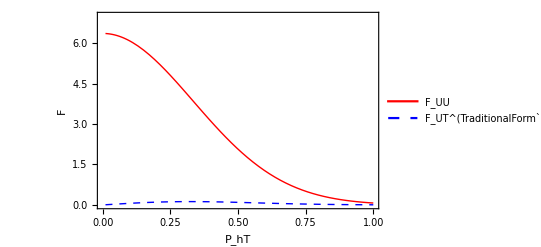

```mathematica
x=0.1;
z=0.3;
Q2=2.;

Plot[{FUUnnpss["pi+",x,z,Q2,PhT],FUTf1tperpnnpss["pi+",x,z,Q2,PhT]},{PhT,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,7}},PlotStyle->{{Thick,Red},{Thick,Dashed,Blue}}, FrameLabel->{"P_hT","F"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"F_UU","F_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},{0.7,0.7}]]

Clear[x,z,Q2];
```

## A_UT^sin[Φ_h-Φ_S]numerics:

```mathematica
AUTSiversnnpss[pion_,x_,z_,Q2_,PT_] := FUTf1tperpnnpss[pion,x,z,Q2,PT]/FUUnnpss[pion,x,z,Q2,PT];
```

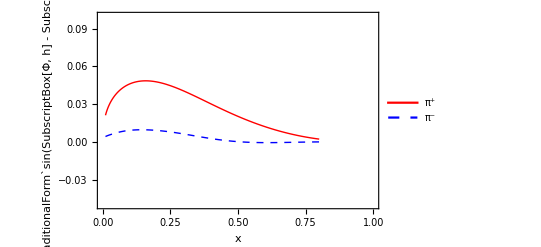

```mathematica
x=0.1;
z=0.3;
Q2=2.;
PT=0.5;
AUTSiverspipplot = Plot[{AUTSiversnnpss["pi+",x,z,Q2,PT] ,AUTSiversnnpss["pi-",x,z,Q2,PT] },{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.7}]]
Clear[x,z,Q2,PT];
```

Phenomenology of leading twist single spin asymmetry A_UT^sin[Φ_h+Φ_S]Collins Asymmetry

## F_UT^sin[Φ_h+Φ_S] analytical result:

```mathematica
Print["Eq(2.18 c)  C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp]"  ]
PTweightUTh1[kt_] := 1;
```

Eq(2.18 c)  C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp]

```mathematica
Print["Eq(2.18 c)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]])= C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp] ="  ]
ConvolutionTMD[omega1A,h1,H1perp]
```

Eq(2.18 c)  F_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]])= C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp] =

(2 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1^2 z^2)) H_1^(FIRST perp) hh_1 M_hadron P_hT z)/(π (p_TCOLLINS^2+k_Th1^2 z^2)^2)

```mathematica
Print["Eq(2.18 c)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp] ="  ]
PTConvolutionTMD[PTweightUTh1,omega1A,h1,H1perp]
```

Eq(2.18 c)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[SubscriptBox[Φ, h] + SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ (h̄)/(z SubscriptBox[M, h]) h_1 H_(1  T)^perp] =

(H_1^(FIRST perp) hh_1 M_hadron √π z)/(√(p_TCOLLINS^2+k_Th1^2 z^2))

## F_UT^sin[Φ_h+Φ_S] numerics:

```mathematica
(*Eq. 5.8a*)
avUTPTh1[z_]:= avp MC^2/(avp+MC^2)+avk z^2;

GUTh1[z_,PT_] := Mp^2/(π avUTPTh1[z]^2) Exp[(-PT^2/avUTPTh1[z])]
AUTh1[z_] := (Mh z √π)/(√avUTPTh1[z])  

FUTh1[pion_,x_,z_,Q2_,PT_] := (2z PT Mh)/Mp^2((4.0/9.0)h1u[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1d[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GUTh1[z,PT]

(*Eq. 5.8b*)
FUTh1Integrated[pion_,x_,z_,Q2_] := ((4.0/9.0)h1u[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1d[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AUTh1[z]
```

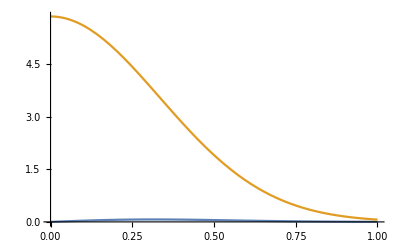

```mathematica
Plot[{FUTh1["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UT^sin[Φ_h+Φ_S]numerics:

```mathematica
AUTCollins[pion_,x_,z_,Q2_,PT_] := FUTh1[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUTCollinsIntegrated[pion_,x_,z_,Q2_] := FUTh1Integrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of PT dependence

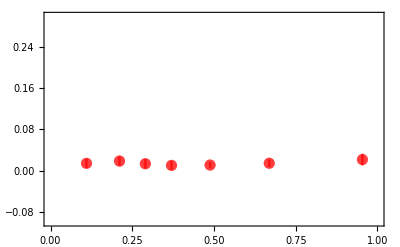

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pip_pt_lba_10.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[5]],data[[i]][[6]]},ErrorBar[Sqrt[data[[i]][[7]]^2+data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

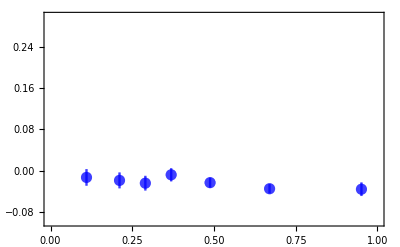

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pim_pt_lba_10.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[5]],data[[i]][[6]]},ErrorBar[Sqrt[data[[i]][[7]]^2+data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
AUTCollinspimfuncPT[PT_] :=AUTCollins["pi-",0.1,0.34,2.4, PT];
AUTCollinspipfuncPT[PT_] :=AUTCollins["pi+",0.1,0.34,2.4, PT];
```

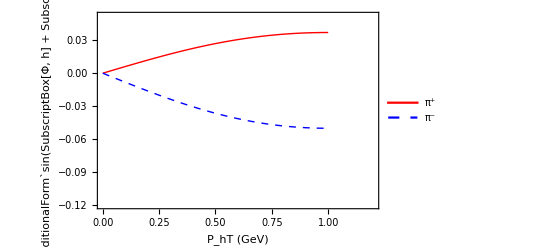

```mathematica
AUTCollinspipplotPT = Plot[{AUTCollinspipfuncPT[PT],AUTCollinspimfuncPT[PT]},{PT,0,1.},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1.2},{-0.12,0.052}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] + SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

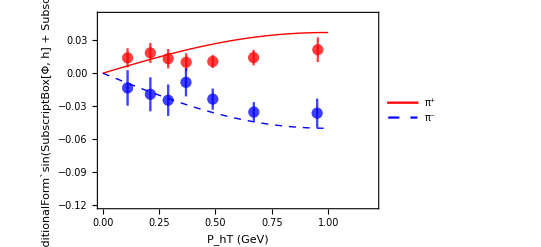

```mathematica
Show[AUTCollinspipplotPT,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUTCollins_PT.pdf",%,Background->None]
```

../tex/figs/AUTCollins_PT.pdf

### Plot of x dependence

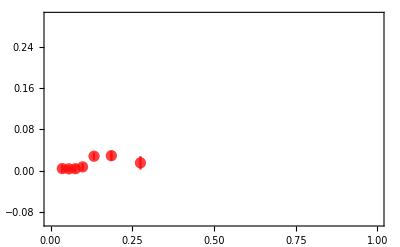

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pip_x_lba_10.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[2]],data[[i]][[6]]},ErrorBar[Sqrt[data[[i]][[7]]^2+data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

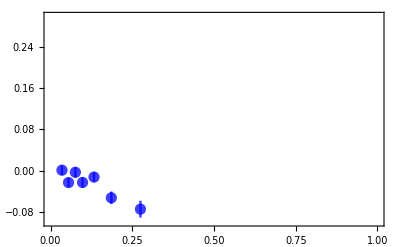

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pim_x_lba_10.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[2]],data[[i]][[6]]},ErrorBar[Sqrt[data[[i]][[7]]^2+data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
AUTXCollinspipfunc[x_] :=AUTCollinsIntegrated["pi+",x,0.34,2.4];
```

```mathematica
AUTCollinspimfunc[x_] :=AUTCollinsIntegrated["pi-",x,0.34,2.4];
```

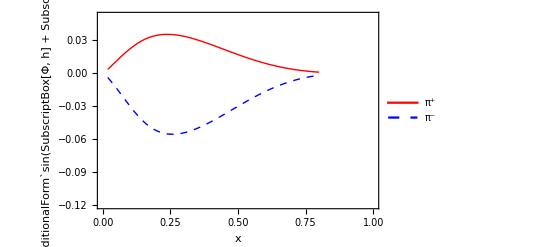

```mathematica
AUTCollinspipplot = Plot[{AUTXCollinspipfunc[x] ,AUTCollinspimfunc[x] },{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.12,0.052}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] + SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.17}]]
```

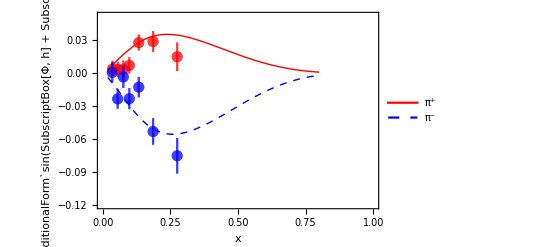

```mathematica
Show[AUTCollinspipplot,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUTCollins_x.pdf",%,Background->None]
```

../tex/figs/AUTCollins_x.pdf

### Plot of x dependence COMPASS

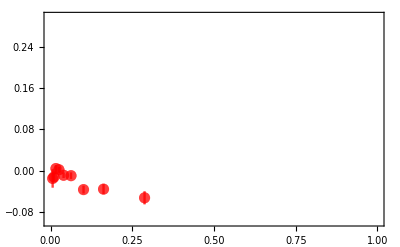

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pip_x_compass_proton_14.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[4]],data[[i]][[7]]},ErrorBar[Sqrt[data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

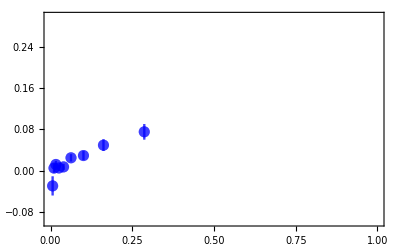

```mathematica
Clear[data,tab];
data=Cases[Import["./data/collins_aut_pim_x_compass_proton_14.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[4]],data[[i]][[7]]},ErrorBar[Sqrt[data[[i]][[8]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
AUTXCollinspipfunc[x_] :=AUTCollinsIntegrated["pi+",x,0.34,2.4];
```

```mathematica
AUTCollinspimfunc[x_] :=AUTCollinsIntegrated["pi-",x,0.34,2.4];
```

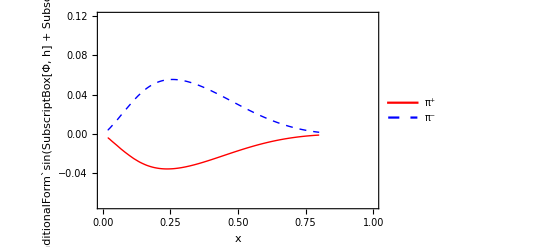

```mathematica
AUTCollinspipplot = Plot[{(-1)*AUTXCollinspipfunc[x] ,(-1)*AUTCollinspimfunc[x] },{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.072,0.12}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","-A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] + SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.67}]]
```

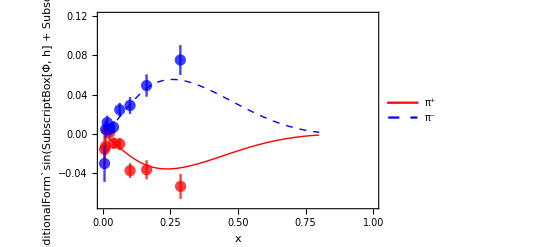

```mathematica
Show[AUTCollinspipplot,plotdataCOMPASSpip,plotdataCOMPASSpim]
```

```mathematica
Export["../tex/figs/AUTCollins_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUTCollins_COMPASS_x.pdf

Phenomenology of leading twist single spin asymmetry A_UT^sin[3 Φ_h-Φ_S]Pretzelosity  Asymmetry

## F_UT^sin[3 Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(2.18 h)  C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp]"  ]  
PTweightUTh1tp[PhT_] :=1;
```

Eq(2.18 h)  C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp]

```mathematica
Print["Eq(2.18 h)  F_UT^(TraditionalForm`sin[3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp] ="  ]
ConvolutionTMD[omega3,h1Tperp,H1perp]
```

Eq(2.18 h)  F_UT^(TraditionalForm`sin[3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp] =

(2 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_TPRETZELOSITY^2 z^2)) H_1^(FIRST perp) h_T^(perp Second) M^2 M_hadron P_hT^3 z^3)/(π (p_TCOLLINS^2+k_TPRETZELOSITY^2 z^2)^4)

```mathematica
Print["Eq(2.18 h)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp] ="  ]
PTConvolutionTMD[PTweightUTh1tp,omega3,h1Tperp,H1perp]
```

Eq(2.18 h)  ∫ⅆ^2P_hTF_UT^(TraditionalForm`sin[3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ -(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (SubscriptBox[k, T] . SubscriptBox[p, T]) + SubsuperscriptBox[k, T, 2] (OverscriptBox[h, _] . SubscriptBox[p, T]) - 4 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] (OverscriptBox[h, _] . SubscriptBox[p, T]))/(2  z SuperscriptBox[M, 2] SubscriptBox[M, h]) h_(1  T)^perpH_1^perp] =

## F_UT^sin[3 Φ_h-Φ_S] numerics:

```mathematica
(*Eq. 5.10a*)
avkP = avk MTT^2/(avk+MTT^2);
avUTPTh1tp[z_]:= avp MC^2/(avp+MC^2)+avkP z^2;

GUTh1tp[z_,PT_] := (Mp^4 Mh)/(π avUTPTh1tp[z]^4) Exp[(-PT^2/avUTPTh1tp[z])]
AUTh1tp[z_] := (3 Mh Mp^2 z^3 √π)/(2 √(avUTPTh1tp[z]^3))  
FUTh1tp[pion_,x_,z_,Q2_,PT_] := (2 z^3 PT^3)/Mp^2((4.0/9.0)h1TperpuSecondMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1TperpdSecondMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GUTh1tp[z,PT]

(*Eq. 5.10b*)
FUTh1tpIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)h1TperpuSecondMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1TperpdSecondMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AUTh1tp[z]
```

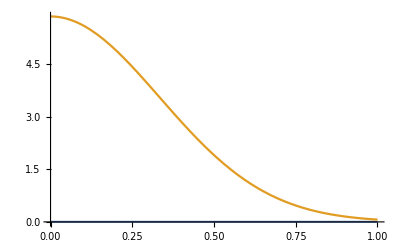

```mathematica
Plot[{FUTh1tp["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UT^sin[3 Φ_h-Φ_S]numerics:

```mathematica
AUTh1tp[pion_,x_,z_,Q2_,PT_] := FUTh1tp[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUTh1tpIntegrated[pion_,x_,z_,Q2_] := FUTh1tpIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of PT dependence

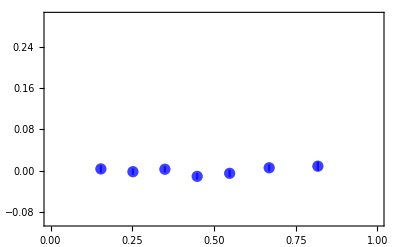

```mathematica
Clear[data,tab];
data=Cases[Import["./data/pretzelosity_compass_proton_hm_pt_13.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[5]],data[[i]][[6]]},ErrorBar[data[[i]][[7]]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

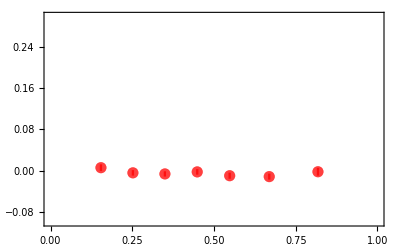

```mathematica
Clear[data,tab];
data=Cases[Import["./data/pretzelosity_compass_proton_hp_pt_13.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[5]],data[[i]][[6]]},ErrorBar[data[[i]][[7]]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
AUTh1tppimfuncPT[PT_] :=AUTh1tp["pi-",0.05,0.35,3.6, PT];
AUTh1tppipfuncPT[PT_] :=AUTh1tp["pi+",0.05,0.35,3.6, PT];
```

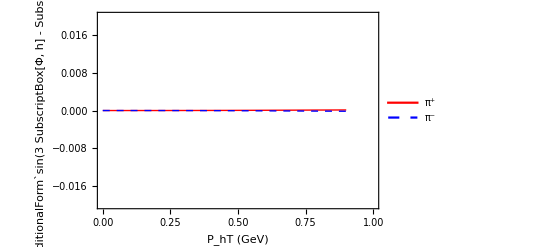

```mathematica
AUTh1tppipplotPT = Plot[{AUTh1tppipfuncPT[PT],AUTh1tppimfuncPT[PT]},{PT,0,0.9},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.02,0.02}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UT^(TraditionalForm`sin(3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

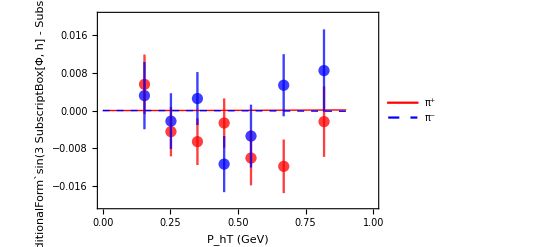

```mathematica
Show[AUTh1tppipplotPT,plotdataCOMPASSpip,plotdataCOMPASSpim]
```

```mathematica
Export["../tex/figs/AUTPretzelosity_PT.pdf",%,Background->None]
```

../tex/figs/AUTPretzelosity_PT.pdf

### Plot of x dependence COMPASS

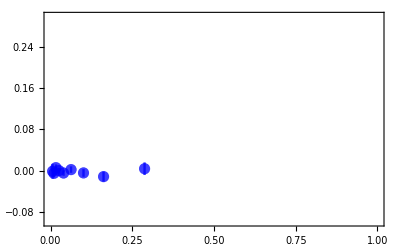

```mathematica
Clear[data,tab];
data=Cases[Import["./data/pretzelosity_compass_proton_hm_x_13.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[6]]},ErrorBar[data[[i]][[7]]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

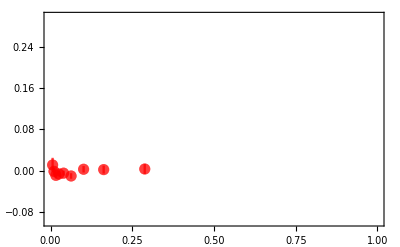

```mathematica
Clear[data,tab];
data=Cases[Import["./data/pretzelosity_compass_proton_hp_x_13.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[6]]},ErrorBar[data[[i]][[7]]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

```mathematica
(*based on numbers from Bakur*)
 
PlotCOMPASS[func_,pion_,color_,file_] := {



Clear[data];
data=Cases[Import["./data/pretzelosity_compass_proton_hm_x_13.dat","Table"],{_?NumberQ,___}]; 
npt = Length[data];

central = Table[{0,0},npt];
 

For[i=1,i≤npt,i++,
xcom = data[[i]][[1]];
ycom = data[[i]][[2]] ;
zcom = data[[i]][[4]] ;
PTcom = data[[i]][[5]] ;
Wcom = 0 ;
Q2com = data[[i]][[2]] ;


central[[i,1]] =  xcom;

central[[i,2]] =  func[pion,xcom,zcom,Q2com];

 
];
(*plotting here*)
Export[file,central,"CSV"];
ListPlot[{central},PlotRange->All,Frame-> False,PlotStyle->{{Thick,color}}, Joined-> True,InterpolationOrder->4]


};
```

```mathematica
AUTh1tppipfunc[x_] :=AUTh1tpIntegrated["pi+",x,0.35,3.6];
```

```mathematica
AUTh1tppimfunc[x_] :=AUTh1tpIntegrated["pi-",x,0.35,3.6];
```

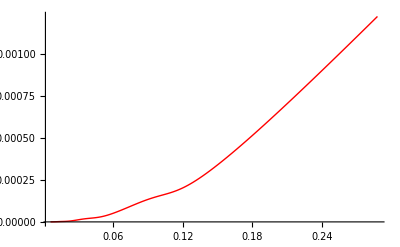

```mathematica
plotpip = PlotCOMPASS[AUTh1tpIntegrated,"pi+",Red,"./bakur/AUTpretzelosity_compass_x_pip.csv"]
```

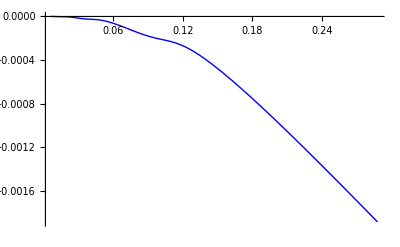

```mathematica
plotpim = PlotCOMPASS[AUTh1tpIntegrated,"pi-",Blue,"./bakur/AUTpretzelosity_compass_x_pim.csv"]
```

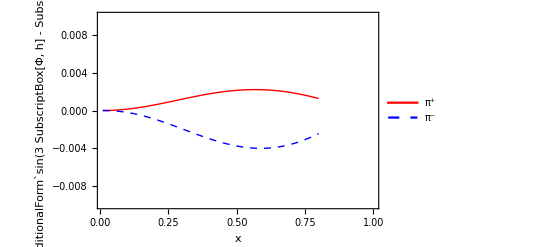

```mathematica
AUTh1tppipplot = Plot[{AUTh1tppipfunc[x],AUTh1tppimfunc[x]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0.01,1},{-0.01,0.01}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.78}]]
```

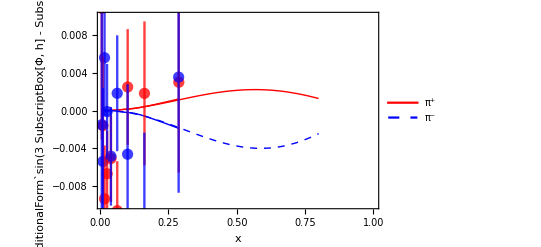

```mathematica
Show[AUTh1tppipplot,plotpip,plotpim,plotdataCOMPASSpip,plotdataCOMPASSpim]
```

```mathematica
Show[AUTh1tppipplot]
```

-Graphics-

```mathematica
Export["../tex/figs/AUTPretzelosity_x.pdf",%,Background->None]
```

../tex/figs/AUTPretzelosity_x.pdf

Phenomenology of leading twist single spin asymmetry A_UU^cos[2 Φ_h]Boer-Mulders Asymmetry

## F_UU^cos[2 Φ_h] analytical result:

```mathematica
Print["Eq(2.18 f)  C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp]"  ]
PTweightUTh1perp[kt_] := 1;
```

Eq(2.18 f)  C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp]

```mathematica
Print["Eq(...)  F_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])= C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp] ="  ]
ConvolutionTMD[omega2AB,h1perp,H1perp]
```

Eq(...)  F_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])= C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_BOERMULDERS^2 z^2)) H_1^(FIRST perp) h_1^(FIRST perp) M M_hadron P_hT^2 z^2)/(π (p_TCOLLINS^2+k_BOERMULDERS^2 z^2)^3)

```mathematica
Print["Eq(...)  ∫ⅆ^2P_hTF_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])=∫ⅆ^2P_hT C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp] ="  ]
PTConvolutionTMD[PTweightUTh1perp,omega2AB,h1perp,H1perp]
```

Eq(...)  ∫ⅆ^2P_hTF_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])=∫ⅆ^2P_hT C[ (2 (OverscriptBox[h, _] . SubscriptBox[p, T]) (OverscriptBox[h, _] . SubscriptBox[k, T]) - (SubscriptBox[p, T] . SubscriptBox[k, T]))/(z M SubscriptBox[M, h]) h_1^perp H_(1  T)^perp] =

(4 H_1^(FIRST perp) h_1^(FIRST perp) M M_hadron z^2)/(p_TCOLLINS^2+k_BOERMULDERS^2 z^2)

## F_UU^cos[2 Φ_h] numerics:

```mathematica
(*Eq. 5.9a*)
avc = MC^2 avp/(MC^2 + avp);
avUUcos2phiPT[z_]:= avc+avkBM z^2;

GfactorUUcos2phi[z_,PT_] := (4 Mp^3 Mh)/(π avUUcos2phiPT[z]^3) Exp[(-PT^2/avUUcos2phiPT[z])]
AfactorUUcos2phi[z_] := (4 Mh Mp z^2)/avUUcos2phiPT[z]  

FUUcos2phi[pion_,x_,z_,Q2_,PT_] := (z^2 PT^2)/Mp^2((4.0/9.0)h1perpuFirstMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2]+(1.0/9.0)h1perpdFirstMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GfactorUUcos2phi[z,PT]

(*Eq. 5.9b*)
FUUcos2phiIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)h1perpuFirstMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1perpdFirstMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AfactorUUcos2phi[z]
```

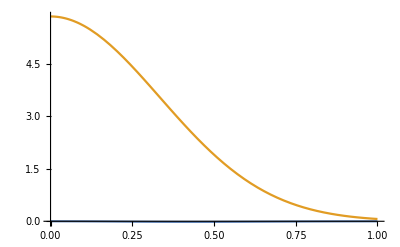

```mathematica
Plot[{FUUcos2phi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UU^cos[2 Φ_h]numerics:

```mathematica
AUUcos2phi[pion_,x_,z_,Q2_,PT_] := FUUcos2phi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUUcos2phiIntegrated[pion_,x_,z_,Q2_] := FUUcos2phiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of pt dependence

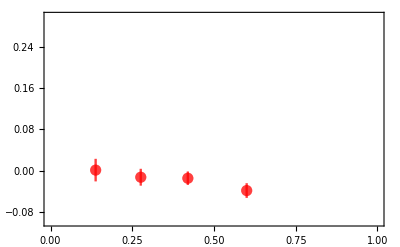

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_hermes_hp_pt.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]^2+data[[i]][[4]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

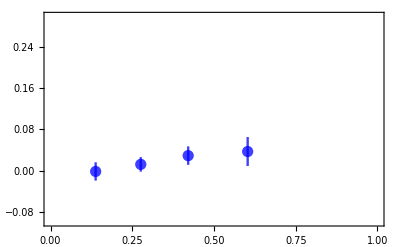

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_hermes_hm_pt.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]^2+data[[i]][[4]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

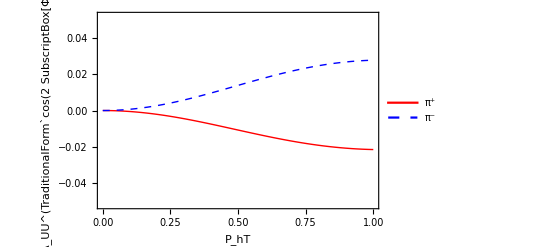

```mathematica
AUTBMlot = Plot[{AUUcos2phi["pi+",0.1,0.34,2.4,PT],AUUcos2phi["pi-",0.1,0.34,2.4,PT]},{PT,0,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.052,0.052}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT","A_UU^(TraditionalForm`cos(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.12,0.8}]]
```

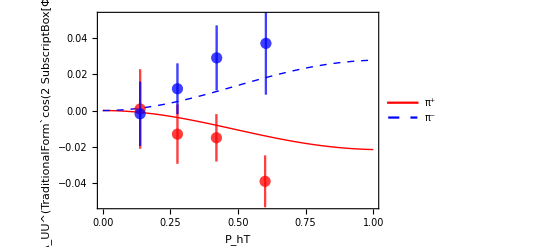

```mathematica
Show[AUTBMlot,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUUcos2phi_PT.pdf",%,Background->None]
```

../tex/figs/AUUcos2phi_PT.pdf

### Plot of x dependence

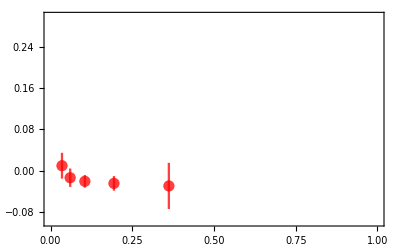

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_hermes_hp_x.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]^2+data[[i]][[4]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

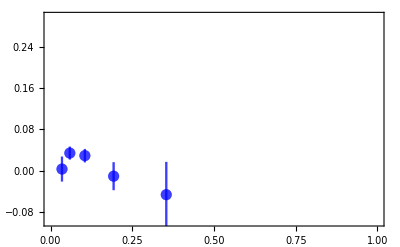

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_hermes_hm_x.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[2]]},ErrorBar[Sqrt[data[[i]][[3]]^2+data[[i]][[4]]^2]]},{i,Length[data]},{j,1}];
plotdataHERMESpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

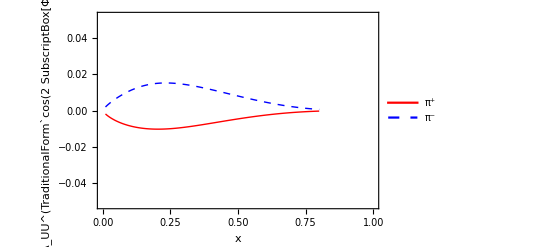

```mathematica
AUTBMlot = Plot[{AUUcos2phiIntegrated["pi+",x,0.34,2.4],AUUcos2phiIntegrated["pi-",x,0.34,2.4]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.052,0.052}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UU^(TraditionalForm`cos(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.7}]]
```

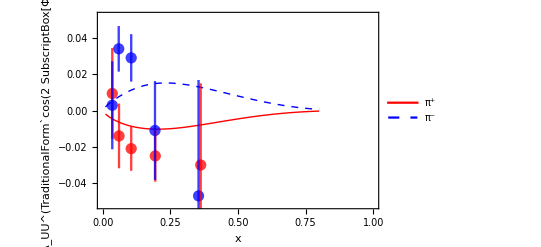

```mathematica
Show[AUTBMlot,plotdataHERMESpip,plotdataHERMESpim]
```

```mathematica
Export["../tex/figs/AUUcos2phi_x.pdf",%,Background->None]
```

../tex/figs/AUUcos2phi_x.pdf

### Plot of x dependence COMPASS

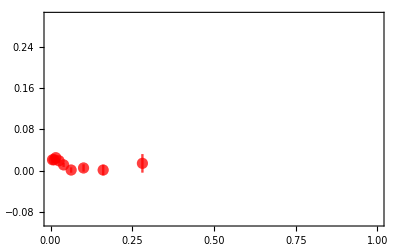

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_compass_hp_x.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[10]]},ErrorBar[Sqrt[data[[i]][[11]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMPASSpip=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

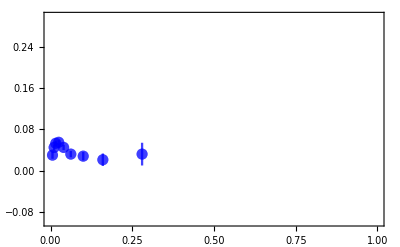

```mathematica
Clear[data,tab];
data=Cases[Import["./data/boermulders_compass_hm_x.dat","Table"],{_?NumberQ,___}]; 
tab =  Table[{{data[[i]][[1]],data[[i]][[10]]},ErrorBar[Sqrt[data[[i]][[11]]^2]]},{i,Length[data]},{j,1}];
plotdataCOMOASSpim=ErrorListPlot[tab, Frame-> True,PlotRange->{{0,1.},{-0.1,0.3}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

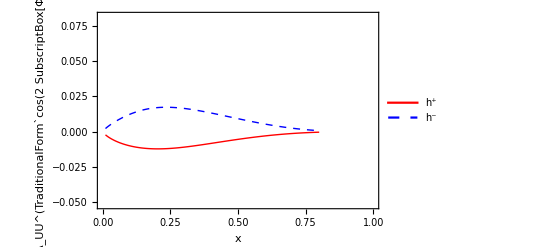

```mathematica
AUTBMlot = Plot[{AUUcos2phiIntegrated["pi+",x,0.37,2.4],AUUcos2phiIntegrated["pi-",x,0.37,2.4]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.052,0.082}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UU^(TraditionalForm`cos(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"h^+","h^-"},{0.7,0.7}]]
```

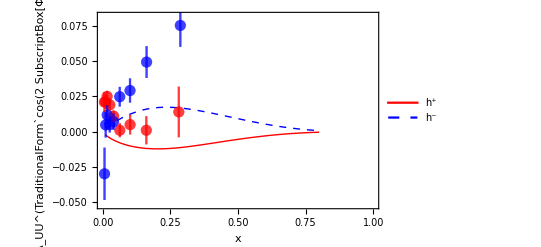

```mathematica
Show[AUTBMlot,plotdataCOMPASSpip,plotdataCOMPASSpim]
```

```mathematica
Export["../tex/figs/AUUcos2phi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUUcos2phi_COMPASS_x.pdf

## F_UU^cos[2 Φ_h] twist-4 analytical result:

```mathematica
Print["Eq()  2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1]"  ]
weightUTcos2phi1[kt_,PhT_,phi_] := (2 (kt Cos[phi])^2 - kt kt);
PTweightUTcos2phi1[kt_] := 1;
```

Eq()  2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1]

```mathematica
Print["Eq(...)  F_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])= 2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1] ="  ]
2/Q^2 ConvolutionTMD[weightUTcos2phi1,f1,D1]
```

Eq(...)  F_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])= 2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_TA^2 z^2)) f_1 (k_TA^2)^2 P_hT^2 z^2)/(π Q^2 (p_TA^2+k_TA^2 z^2)^3)

```mathematica
Print["Eq(...)  ∫ⅆ^2P_hTF_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])=∫ⅆ^2P_hT 2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1] ="  ]
2/Q^2 PTConvolutionTMD[PTweightUTcos2phi1,weightUTcos2phi1,f1,D1]
```

Eq(...)  ∫ⅆ^2P_hTF_UU^(TraditionalForm`cos[2 SubscriptBox[Φ, h]])=∫ⅆ^2P_hT 2/Q^2C[ (2(h̄.k_T)^2-k_T^2) f_1 D_1] =

(2 D_1 f_1 (k_TA^2)^2 z^2)/(Q^2 (p_TA^2+k_TA^2 z^2))

Phenomenology of leading twist double spin asymmetry A_LT^cos[Φ_h-Φ_S]

## F_LT^cos[Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(2.18 e, 4.1a)  C[ (h̄)/M g_(1  T) D_1]"  ]
PTweightLTg1t[kt_] := 1;
```

Eq(2.18 e, 4.1a)  C[ (h̄)/M g_(1  T) D_1]

```mathematica
Print["Eq(2.18 e)  F_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ (h̄)/M g_(1  T) D_1] ="  ]
ConvolutionTMD[omega1B,g1T,D1]
```

Eq(2.18 e)  F_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ (h̄)/M g_(1  T) D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1T^2 z^2)) g_T^FIRST M P_hT z)/(π (p_TA^2+k_Tg1T^2 z^2)^2)

```mathematica
Print["Eq(2.18 e)  F_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ (h̄)/M g_(1  T) D_1] ="  ]
ConvolutionTMD[omega1B,g1T,D1]
```

Eq(2.18 e)  F_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= C[ (h̄)/M g_(1  T) D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1T^2 z^2)) g_T^FIRST M P_hT z)/(π (p_TA^2+k_Tg1T^2 z^2)^2)

```mathematica
Print["Eq(54)  ∫ⅆ^2P_hTF_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ (h̄)/M g_(1  T) D_1] ="  ]
PTConvolutionTMD[PTweightLTg1t,omega1B,g1T,D1]
```

Eq(54)  ∫ⅆ^2P_hTF_LT^(TraditionalForm`cos[SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT C[ (h̄)/M g_(1  T) D_1] =

ConditionalExpression[D_1 g_T^FIRST M √π z √(1/(p_TA^2+k_Tg1T^2 z^2)),Re[p_TA^2+k_Tg1T^2 z^2]>0]

## F_LT^cos[Φ_h-Φ_S] numerics:

```mathematica
(*Eq. 6.1a*)
avkg1T = avkg; (*assumption*)
avLLPT[z_]:= avp+avkg1T z^2;

GLT[z_,PT_] := (2 Mp^2)/(π avLLPT[z]^2) Exp[(-PT^2/avLLPT[z])]
ALT[z_] := (Mp z √π)/(√avLLPT[z])  

FLT[pion_,x_,z_,Q2_,PT_] := (z PT)/Mp((4.0/9.0)g1Tperpu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1Tperpd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1Tperps[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1Tperpubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1Tperpdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1Tperpsbar[x,Q2] D1sbar[pion,z,Q2] ) GLT[z,PT]

(*Eq. 6.1b*)
FLTIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)g1Tperpu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1Tperpd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1Tperps[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1Tperpubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1Tperpdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1Tperpsbar[x,Q2] D1sbar[pion,z,Q2] ) ALT[z]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.11061486030073391061134824298051171354018151760101318359375}. NIntegrate obtained -0.0262016 and 3.01517×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.120682927156044721150873755277643795125186443328857421875}. NIntegrate obtained -0.169845 and 1.84949×10^-7 for the integral and error estimates.

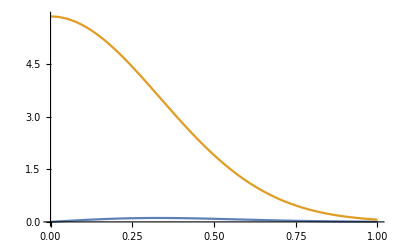

```mathematica
Plot[{FLT["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_LT^cos[Φ_h-Φ_S]numerics:

```mathematica
ALT[pion_,x_,z_,Q2_,PT_] := FLT[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

ALTIntegrated[pion_,x_,z_,Q2_] := FLTIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
ALTCOMpimfunc[x_] :=ALTIntegrated["pi-",x,zcom,Q2com];
ALTCOMpipfunc[x_] :=ALTIntegrated["pi+",x,zcom,Q2com];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained 6.76663 and 0.0000290239 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained -3.72205 and 0.000026918 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained 0.0667851 and 0.0000137262 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

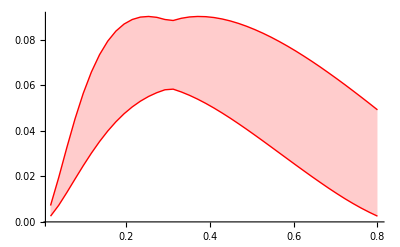

```mathematica
ALTCOMpiperrorband = ErrorBandX[ALTCOMpipfunc,0.02,0.8,40,Red]
```

```mathematica
ErrorBandPrint[ALTCOMpipfunc,0.02,0.8,40,"./bakur/alt_compass_x_pip.csv"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 6.76732 and 0.000028186 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.72263 and 0.0000267306 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.066699 and 0.0000109926 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{./bakur/alt_compass_x_pip.csv}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

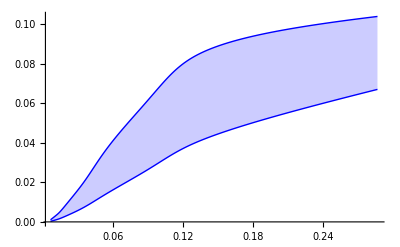

```mathematica
ErrorBandCOMPASS[ALT,"pi+",Blue,"./bakur/alt_compass_x_pip.csv"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained 7.39151 and 0.0000184382 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained -3.89736 and 0.0000238859 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0207719339587382235967627508443911210633814334869384765625}. NIntegrate obtained 0.0867431 and 9.53729×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

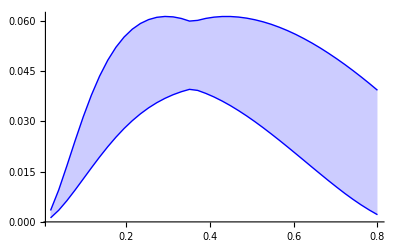

```mathematica
ALTCOMpimerrorband = ErrorBandX[ALTCOMpimfunc,0.02,0.8,40,Blue]
```

```mathematica
ErrorBandPrint[ALTCOMpimfunc,0.02,0.8,40,"./bakur/alt_compass_x_pim.csv"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 7.39237 and 0.0000182997 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained -3.89802 and 0.0000263748 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.020767915025659384846423716197705289232544600963592529296875}. NIntegrate obtained 0.0866683 and 9.20885×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{./bakur/alt_compass_x_pim.csv}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

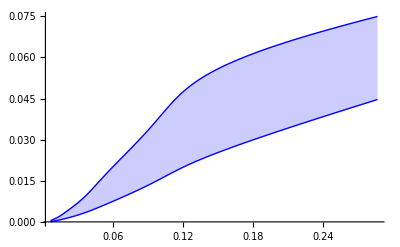

```mathematica
ErrorBandCOMPASS[ALT,"pi-",Blue,"./bakur/alt_compass_x_pim.csv"]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained 6.65261 and 7.0714×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained -3.34458 and 9.58752×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained 0.133589 and 3.08659×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

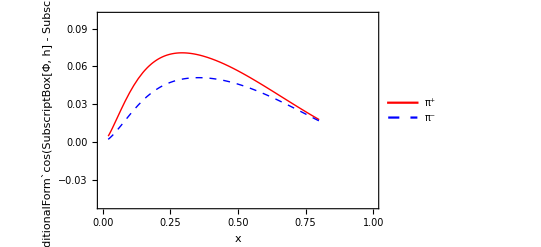

```mathematica
ALTCOMpiplot = Plot[{ALTCOMpipfunc[x],ALTCOMpimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_LT^(TraditionalForm`cos(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

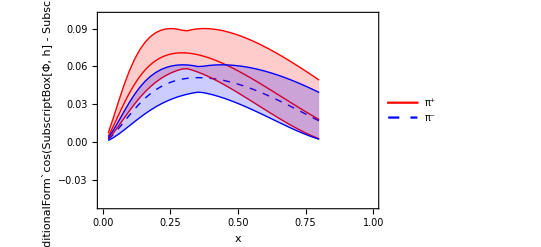

```mathematica
Show[ALTCOMpiplot,ALTCOMpiperrorband,ALTCOMpimerrorband]
```

```mathematica
Export["../tex/figs/ALT_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALT_COMPASS_x.pdf

### Positivity

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 M^2))^1 g1T[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[((g_T^FIRST)^2)/(4 k_Tg1T^2 π),Re[k_Tg1T^2]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 M^2))^1 f1Tperp[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[((f_T^(FIRST perp))^2)/(4 k_TSIVERS^2 π),Re[k_TSIVERS^2]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 M^2))^1 (f1[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[f_1^2/(16 M^2 π),Re[k_TA^2]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 M^2))^1 (g1[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[g_1^2/(16 M^2 π),Re[k_Tg1^2]>0]

```mathematica
Positivityu[x_,Q2_] :=((f1u[x,Q2])/(4 Mp √π)-√((g1u[x,Q2])^2/(16 Mp^2 π)+(f1TperpuFirstMoment[x,Q2])^2/(4 avkBM  π)+(g1Tperpu[x,Q2])^2/(4 avkg1T π)))/((f1u[x,Q2])/(4 Mp √π)+√((g1u[x,Q2])^2/(16 Mp^2 π)+(f1TperpuFirstMoment[x,Q2])^2/(4 avkBM  π)+(g1Tperpu[x,Q2])^2/(4 avkg1T π)))
```

```mathematica
Positivityd[x_,Q2_] :=((f1d[x,Q2])/(4 Mp √π)-√((g1d[x,Q2])^2/(16 Mp^2 π)+(f1TperpdFirstMoment[x,Q2])^2/(4 avkBM  π)+(g1Tperpd[x,Q2])^2/(4 avkg1T π)))/((f1d[x,Q2])/(4 Mp √π)+√((g1d[x,Q2])^2/(16 Mp^2 π)+(f1TperpdFirstMoment[x,Q2])^2/(4 avkBM  π)+(g1Tperpd[x,Q2])^2/(4 avkg1T π)))
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained 5.76795 and 0.000010212 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0303080265665682836717653714231346384622156620025634765625}. NIntegrate obtained -3.12102 and 0.0000117033 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

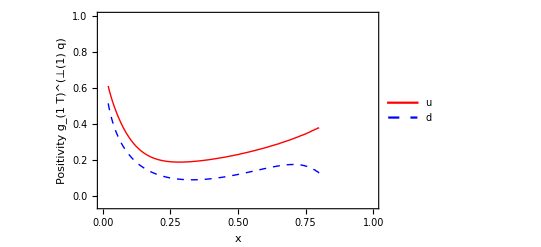

```mathematica
ALTCOMpiplot = Plot[{Positivityu[x,2.4],Positivityd[x,2.4]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,1.}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","Positivity g_(1  T)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"u","d"},{0.7,0.55}]]
```

```mathematica
Export["../tex/figs/g1t_positivity.pdf",%,Background->None]
```

../tex/figs/g1t_positivity.pdf

Phenomenology of leading twist double spin asymmetry A_UL^sin[2 Φ_S](Kotzinian-Mulders)

## F_UL^sin[2 Φ_h] analytical result:

```mathematica
Print["Eq(2.18 g, 4.1b)  C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp]"  ]
PTweightULsin2phi[PhT_] :=1;
```

Eq(2.18 g, 4.1b)  C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp]

```mathematica
Print["Eq(2.18 g)   F_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]])= C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp] ="  ]
ConvolutionTMD[omega2AB,h1Lperp,H1perp]
```

Eq(2.18 g)   F_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]])= C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1L^2 z^2)) H_1^(FIRST perp) h_L^FIRST M M_hadron P_hT^2 z^2)/(π (p_TCOLLINS^2+k_Th1L^2 z^2)^3)

```mathematica
Print["Eq(2.18 g)  ∫ⅆ^2P_hT F_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp] ="  ]
PTConvolutionTMD[PTweightULsin2phi,omega2AB,h1Lperp,H1perp]
```

Eq(2.18 g)  ∫ⅆ^2P_hT F_UL^(TraditionalForm`sin[2 SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT C[ (2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(z M SubscriptBox[M, h]) h_(1  L)^perpH_1^perp] =

(4 H_1^(FIRST perp) h_L^FIRST M M_hadron z^2)/(p_TCOLLINS^2+k_Th1L^2 z^2)

## F_UL^sin[2 Φ_h] numerics:

```mathematica
(*Eq. 6.2a*)
avc = MC^2 avp/(MC^2 + avp);
avkh1l = avk; (* assumption *)
avULsin2phiPT[z_]:= avc+avkh1l z^2;

GfactorULsin2phi[z_,PT_] := (4 Mp^3 Mh)/(π avULsin2phiPT[z]^3) Exp[(-PT^2/avULsin2phiPT[z])]
AfactorULsin2phi[z_] := (4 Mh Mp z^2)/avULsin2phiPT[z]  

FULsin2phi[pion_,x_,z_,Q2_,PT_] := (z^2 PT^2)/Mp^2((4.0/9.0)h1Lu[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1Ld[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GfactorULsin2phi[z,PT]

(*Eq. 6.2b*)
FULsin2phiIntegrated[pion_,x_,z_,Q2_] := ((4.0/9.0)h1Lu[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1Ld[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AfactorULsin2phi[z]
```

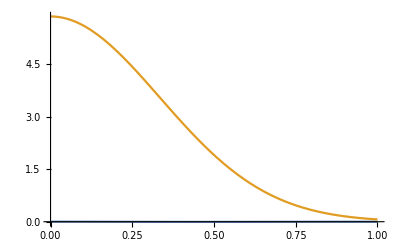

```mathematica
Plot[{FULsin2phi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UL^sin[2 Φ_h]numerics:

```mathematica
AULsin2phi[pion_,x_,z_,Q2_,PT_] := FULsin2phi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AULsin2phiIntegrated[pion_,x_,z_,Q2_] := FULsin2phiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS NEW

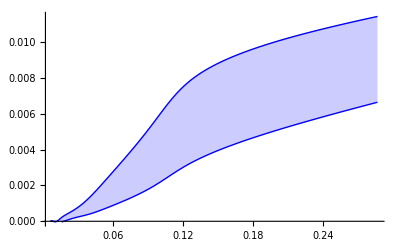

```mathematica
AULsin2phipimerrorband =ErrorBandCOMPASS[AULsin2phi,"pi-",Blue,"./bakur/AULsin2phi_compass_x_pim.csv"]
centralpim = central;
```

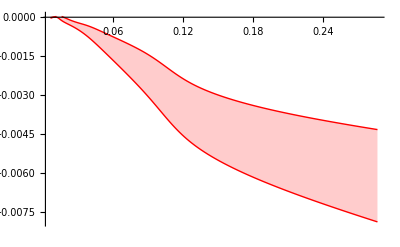

```mathematica
AULsin2phipiperrorband =ErrorBandCOMPASS[AULsin2phi,"pi+",Red,"./bakur/AULsin2phi_compass_x_pip.csv"]
centralpip = central;
```

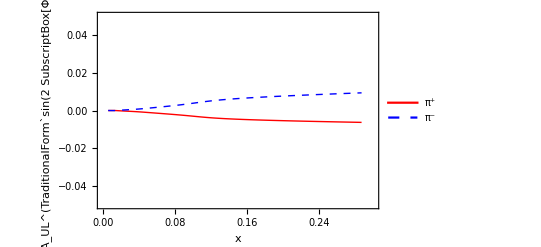

```mathematica
AULsin2phipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UL^(TraditionalForm`sin(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

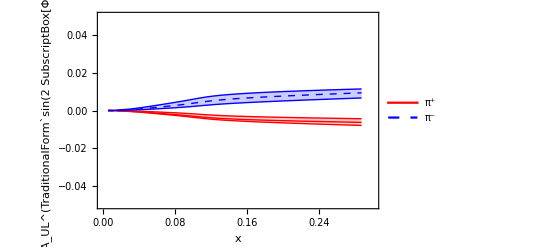

```mathematica
Show[AULsin2phipiplot,AULsin2phipiperrorband,AULsin2phipimerrorband]
```

```mathematica
Export["../tex/figs/AULsin2phi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AULsin2phi_COMPASS_x.pdf

### Positivity

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 M^2))^1 h1Lperp[kt^2])^2 ⅆphiⅆkt
```

((h_L^FIRST)^2)/(4 k_Th1L^2 π)

```mathematica
∫_0^∞ ∫_0^(2 π) kt((kt^2/(2 M^2))^1 h1perp[kt^2])^2 ⅆphiⅆkt
```

((h_1^(FIRST perp))^2)/(4 k_BOERMULDERS^2 π)

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 M^2))^1 (f1[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[f_1^2/(16 M^2 π),Re[k_TA^2]>0]

```mathematica
∫_0^∞ ∫_0^(2 π) kt(kt^2/(4 M^2))^1 (g1[kt^2])^2 ⅆphiⅆkt
```

ConditionalExpression[g_1^2/(16 M^2 π),Re[k_Tg1^2]>0]

```mathematica
Positivityu[x_,Q2_] := ((f1u[x,Q2])/(4 Mp √π)-√((g1u[x,Q2])^2/(16 Mp^2 π)+(h1perpuFirstMoment[x,Q2])^2/(4 avks  π)+(h1Lu[x,Q2])^2/(4 avkg1T π)))/((f1u[x,Q2])/(4 Mp √π)+√((g1u[x,Q2])^2/(16 Mp^2 π)+(h1perpuFirstMoment[x,Q2])^2/(4 avks  π)+(h1Lu[x,Q2])^2/(4 avkg1T π)))
```

```mathematica
Positivityd[x_,Q2_] :=((f1d[x,Q2])/(4 Mp √π)-√((g1d[x,Q2])^2/(16 Mp^2 π)+(h1perpdFirstMoment[x,Q2])^2/(4 avks  π)+(h1Ld[x,Q2])^2/(4 avkg1T π)))/((f1d[x,Q2])/(4 Mp √π)+√((g1d[x,Q2])^2/(16 Mp^2 π)+(h1perpdFirstMoment[x,Q2])^2/(4 avks  π)+(h1Ld[x,Q2])^2/(4 avkg1T π)))
```

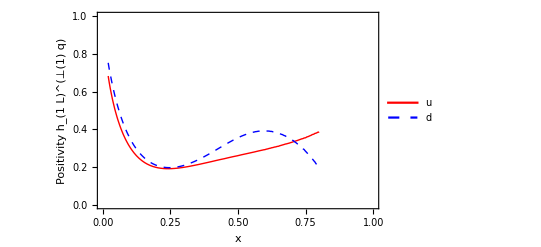

```mathematica
AULsin2phipiplot = Plot[{Positivityu[x,2.4],Positivityd[x,2.4]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0.,1.}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","Positivity h_(1  L)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"u","d"},{0.7,0.55}]]
```

```mathematica
Export["../tex/figs/h1lperp_positivity.pdf",%,Background->None]
```

../tex/figs/h1lperp_positivity.pdf

## A_UL^sin[2 Φ_h]numerics JLab:

### Plot of x dependence

```mathematica
sjlab = Mp^2 + 2 5.7 Mp; 
Clear[x,y,z,Q2,PT]; 
y[Q2_,x_] :=  Q2/(sjlab x);

AULsin2phiY[pion_,x_,z_,Q2_,PT_] := (2(1- y[Q2,x] )FULsin2phi[pion,x,z,Q2,PT])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUU[pion,x,z,Q2,PT])  ;

AULsin2phiIntegratedY[pion_,x_,z_,Q2_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsin2phiIntegrated[pion,x,z,Q2])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUUIntegrated[pion,x,z,Q2]);
```

```mathematica
AULsin2phi0funcY[x_] :=(AULsin2phiY["pi+",x,0.5,2.,0.4]+AULsin2phiY["pi-",x,0.5,2.,0.4])/2;
```

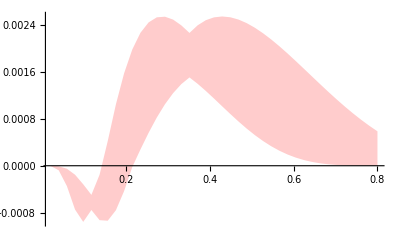

```mathematica
AULsin2phi0errorbandY = ErrorBand[AULsin2phi0funcY,0.02,0.8,40,Red]
```

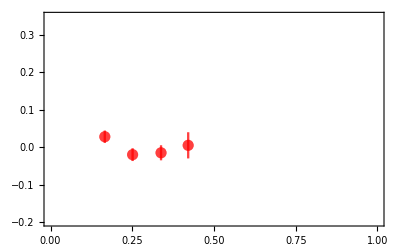

```mathematica
Clear[data,tab];
datapi0=Cases[Import["./data/pi0-eg1dvcs/pi0-aul-sin2-x-dep4.dat","Table"],{_?NumberQ,___}]; 
tabpi0 =  Table[{{datapi0[[i]][[3]],datapi0[[i]][[4]]},ErrorBar[Sqrt[datapi0[[i]][[5]]^2+datapi0[[i]][[6]]^2]]},{i,1,4(*Length[datapip]*)},{j,1}];
plotdataAULpi0=ErrorListPlot[tabpi0, Frame-> True,PlotRange->{{0,1},{-0.2,0.35}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

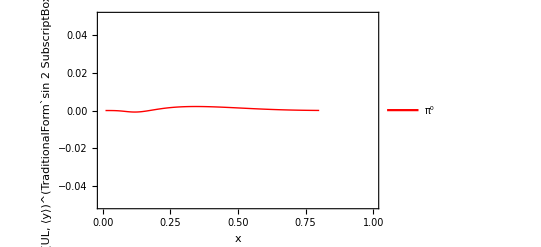

```mathematica
AULsin2philotY = Plot[{AULsin2phi0funcY[x]},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_(UL, ⟨y⟩)^(TraditionalForm`sin 2 SubscriptBox[Φ, h])"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^0"},{0.7,0.7}]]
```

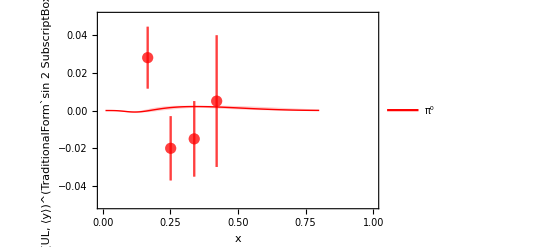

```mathematica
Show[AULsin2philotY,plotdataAULpi0,AULsin2phi0errorbandY]
```

```mathematica
Export["../tex/figs/AULsin2phi_JLAB_x.pdf",%,Background->None]
```

../tex/figs/AULsin2phi_JLAB_x.pdf

## Sub-leading Structure Functions and Asymmetries

Phenomenology of sub-leading twist double spin asymmetry A_LT^cos[Φ_S]

## F_LT^cos[Φ_S] analytical result:

```mathematica
Print["Eq(4.2 b)(2 M)/QC[ -x g_TD_1], " ]
PTweightLTcosphiS[PhT_] :=1;
```

Eq(4.2 b)(2 M)/QC[ -x g_TD_1],

```mathematica
Print["Eq()   F_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]])= (2 M)/QC[ -x g_TD_1] ="  ]
(2 M)/Q(-xBj)ConvolutionTMD[omega0,gT,D1]
```

Eq()   F_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]])= (2 M)/QC[ -x g_TD_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1T^2 z^2)) gT M xBj)/(Q (π p_TA^2+k_Tg1T^2 π z^2))

```mathematica
Print["Eq()  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT (2 M)/QC[ -x g_TD_1]] ="  ]
(2 M)/Q(-xBj)PTConvolutionTMD[PTweightLTcosphiS,omega0,gT,D1]
```

Eq()  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT (2 M)/QC[ -x g_TD_1]] =

ConditionalExpression[-(2 D_1 gT M xBj)/Q,Re[p_TA^2+k_Tg1T^2 z^2]>0]

## F_LT^cos[Φ_S] numerics:

```mathematica
(*Eq. 7.2a*)
avLLPT[z_]:= avp+avkg z^2;
GLTCOSPhi[z_,PT_] := 1/(π avLLPT[z]) Exp[(-PT^2/avLLPT[z])]
ALTCOSPhi[z_] := 1.  
(* did I miss x ? See formula x gt ....*) 
FLTcosPhi[pion_,x_,z_,Q2_,PT_] := (-2 Mp x)/Sqrt[Q2]((4.0/9.0)gTu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)gTd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)gTs[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)gTubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)gTdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)gTsbar[x,Q2] D1sbar[pion,z,Q2] ) GLTCOSPhi[z,PT];

(*Eq. 7.2b*)
FLTcosPhiIntegrated[pion_,x_,z_,Q2_] := (-2 Mp x)/Sqrt[Q2]((4.0/9.0)gTu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)gTd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)gTs[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)gTubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)gTdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)gTsbar[x,Q2] D1sbar[pion,z,Q2] ) ALTCOSPhi[z];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.11061486030073391061134824298051171354018151760101318359375}. NIntegrate obtained -0.0262016 and 3.01517×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.120682927156044721150873755277643795125186443328857421875}. NIntegrate obtained -0.169845 and 1.84949×10^-7 for the integral and error estimates.

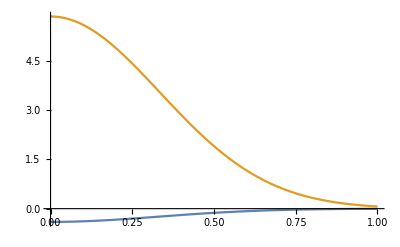

```mathematica
Plot[{FLTcosPhi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_LT^cos[Φ_S]numerics:

```mathematica
ALTcosPhi[pion_,x_,z_,Q2_,PT_] := FLTcosPhi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

ALTcosPhiIntegrated[pion_,x_,z_,Q2_] := FLTcosPhiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS NEW

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

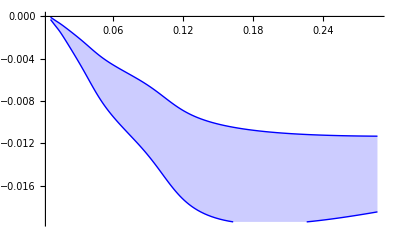

```mathematica
ALTcosPhipimerrorband =ErrorBandCOMPASS[ALTcosPhi,"pi-",Blue,"./bakur/ALTcosPhi_compass_x_pim.csv"]
centralpim = central;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

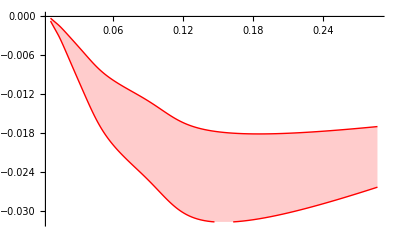

```mathematica
ALTcosPhipiperrorband =ErrorBandCOMPASS[ALTcosPhi,"pi+",Red,"./bakur/ALTcosPhi_compass_x_pip.csv"]
centralpip = central;
```

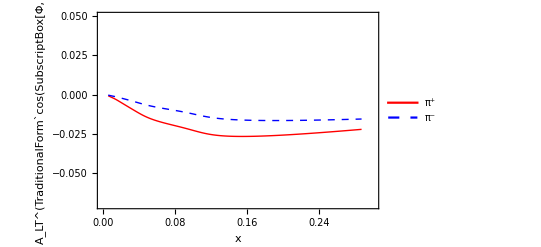

```mathematica
ALTcosPhipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_LT^(TraditionalForm`cos(SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.75}]]
```

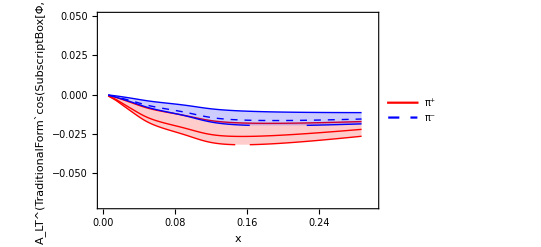

```mathematica
Show[ALTcosPhipiplot,ALTcosPhipiperrorband,ALTcosPhipimerrorband]
```

```mathematica
Export["../tex/figs/ALTcosphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALTcosphi_COMPASS_x.pdf

Phenomenology of sub-leading twist spin asymmetry A_UL^sin[Φ_h]

## F_UL^sin[Φ_h] analytical result:

```mathematica
Clear[x,y,z,Q2,PT]
```

```mathematica
Print["Eq(4.2 e)(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥], x h_L(x) = - 2 h1Lperp(1)(x)" ]
PTweightULsinphih[PhT_] :=1;
```

Eq(4.2 e)(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥], x h_L(x) = - 2 h1Lperp(1)(x)

```mathematica
Print["Eq(4.2 e)   F_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥] ="  ]
(2 M xBj)/Q ConvolutionTMD[omega1A, hL,H1perp]
```

Eq(4.2 e)   F_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_ThL^2 z^2)) H_1^(FIRST perp) hL M M_hadron P_hT xBj z)/(π Q (p_TCOLLINS^2+k_ThL^2 z^2)^2)

```mathematica
Print["Eq(4.2 e)  ∫ⅆ^2P_hT F_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥] ="  ]

(2 M xBj)/Q PTConvolutionTMD[PTweightULsinphih,omega1A, hL,H1perp]
```

Eq(4.2 e)  ∫ⅆ^2P_hT F_UL^(TraditionalForm`sin[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])(x h_L)H_1^⊥] =

ConditionalExpression[(2 H_1^(FIRST perp) hL M M_hadron √π xBj z)/(Q √(p_TCOLLINS^2+k_ThL^2 z^2)),p_TCOLLINS^2+z^2 Re[k_ThL^2]>0]

## F_UL^sin[Φ_h] numerics:

```mathematica
(*Eq. 7.6a*)
avc = MC^2 avp/(MC^2 + avp);
avkh1l = avk; (* assumption *)
avULsinphiPT[z_]:= avc+avkh1l z^2;
(* x hL = h_1L^perp(1) *)
GfactorULsinphi[z_,PT_] := (2 Mp^2)/(π avULsinphiPT[z]^2) Exp[(-PT^2/avULsinphiPT[z])]
AfactorULsinphi[z_] := (Mh z √Pi)/avULsinphiPT[z]^(1/2)  

FULsinphi[pion_,x_,z_,Q2_,PT_] := ((2 Mp)/Sqrt[Q2])(z PT Mh)/Mp^2(-2)((4.0/9.0)h1Lu[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1Ld[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) GfactorULsinphi[z,PT]
(*Eq. 7.6b*)
FULsinphiIntegrated[pion_,x_,z_,Q2_] := ((2 Mp)/Sqrt[Q2])(-2)((4.0/9.0)h1Lu[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1Ld[x,Q2] H1perpFirstMoment["d",pion,z,Q2]) AfactorULsinphi[z]
```

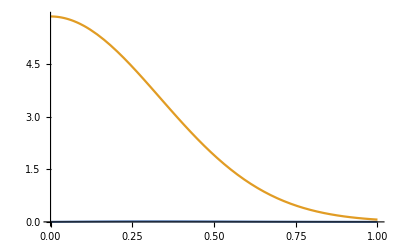

```mathematica
Plot[{FULsinphi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UL^sin[Φ_h]numerics:

```mathematica
AULsinphi[pion_,x_,z_,Q2_,PT_] := FULsinphi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AULsinphiIntegrated[pion_,x_,z_,Q2_] := FULsinphiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS NEW

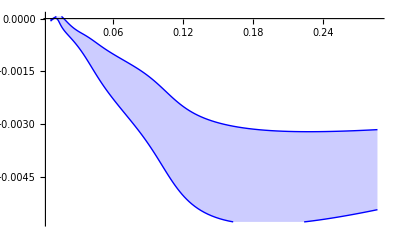

```mathematica
AULsinphipimerrorband =ErrorBandCOMPASS[AULsinphi,"pi-",Blue,"./bakur/AULsinphi_compass_x_pim.csv"]
centralpim = central;
```

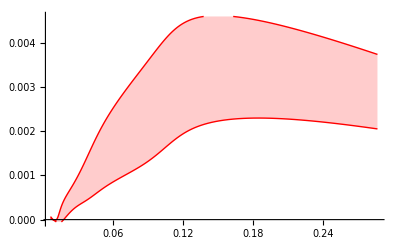

```mathematica
AULsinphipiperrorband =ErrorBandCOMPASS[AULsinphi,"pi+",Red,"./bakur/AULsinphi_compass_x_pip.csv"]
centralpip = central;
```

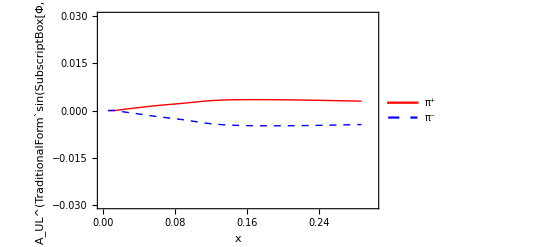

```mathematica
AULsinphipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.03,0.03}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UL^(TraditionalForm`sin(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

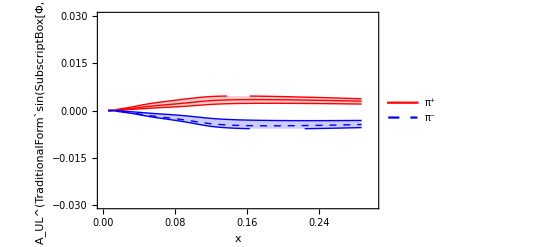

```mathematica
Show[AULsinphipiplot,AULsinphipiperrorband,AULsinphipimerrorband]
```

```mathematica
Export["../tex/figs/AULsinphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AULsinphi_COMPASS_x.pdf

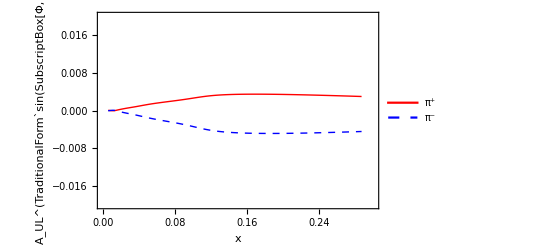

```mathematica
AULsinPhilot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.02,0.02}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UL^(TraditionalForm`sin(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

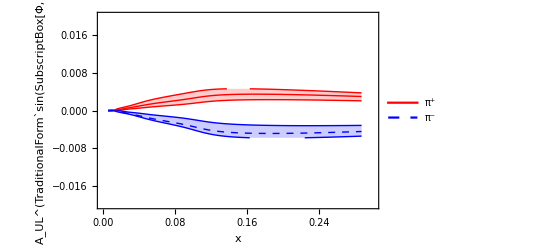

```mathematica
Show[AULsinPhilot,AULsinphipiperrorband,AULsinphipimerrorband]
```

```mathematica
Export["../tex/figs/BAKUR_AULsinphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/BAKUR_AULsinphi_COMPASS_x.pdf

## A_(UL,<y>)^sin[Φ_h]numerics:

### Plot of x dependence

```mathematica
shermes = Mp^2 + 2 27.5 Mp; 
Clear[x,y,z,Q2,PT]; 
y[Q2_,x_] :=  Q2/(shermes x);

AULsinphiY[pion_,x_,z_,Q2_,PT_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsinphi[pion,x,z,Q2,PT])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUU[pion,x,z,Q2,PT])  ;

AULsinphiIntegratedY[pion_,x_,z_,Q2_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsinphiIntegrated[pion,x,z,Q2])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUUIntegrated[pion,x,z,Q2]);

AULsinphiYHERMES[pion_,x_,y_,z_,Q2_,PT_] := ((2- y )√(1-y)FULsinphi[pion,x,z,Q2,PT])/((1-y+1/2 y^2)FUU[pion,x,z,Q2,PT])  ;
```

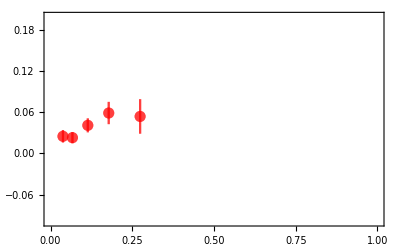

```mathematica
Clear[data,tab];
datapip=Cases[Import["./data/AULsinPhi_hermes_x.dat","Table"],{_?NumberQ,___}]; 
tabpip =  Table[{{datapip[[i]][[1]],datapip[[i]][[12]]},ErrorBar[Sqrt[datapip[[i]][[13]]^2+datapip[[i]][[14]]^2]]},{i,Length[datapip]},{j,1}];
plotdataAULpip=ErrorListPlot[tabpip, Frame-> True,PlotRange->{{0,1},{-0.1,0.2}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

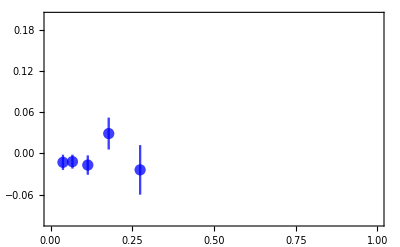

```mathematica
Clear[data,tab];
datapim=Cases[Import["./data/AULsinPhi_hermes_x.dat","Table"],{_?NumberQ,___}]; 
tabpim =  Table[{{datapim[[i]][[1]],datapim[[i]][[15]]},ErrorBar[Sqrt[datapim[[i]][[16]]^2+datapim[[i]][[17]]^2]]},{i,Length[datapim]},{j,1}];
plotdataAULpim=ErrorListPlot[tabpim, Frame-> True,PlotRange->{{0,1},{-0.1,0.2}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

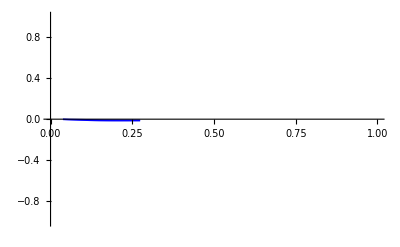

```mathematica
AULsinPhipimerrorbandH =ErrorBandHERMES[AULsinphiYHERMES,"pi-",Blue,"./gunar/AULsinphiYHERMES_x_pim.csv"]
centralpimH = central;
```

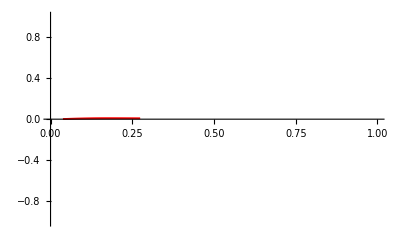

```mathematica
AULsinPhipiperrorbandH =ErrorBandHERMES[AULsinphiYHERMES,"pi+",Red,"./gunar/AULsinphiYHERMES_x_pip.csv"]
centralpipH = central;
```

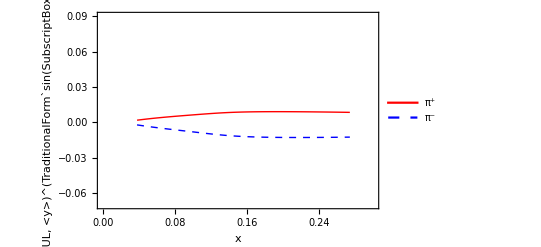

```mathematica
AULsinPhilot = ListPlot[{centralpipH,centralpimH},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.07,0.09}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_(UL, <y>)^(TraditionalForm`sin(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

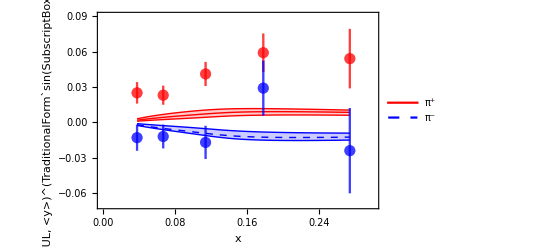

```mathematica
Show[AULsinPhilot,AULsinPhipiperrorbandH,AULsinPhipimerrorbandH,plotdataAULpip,plotdataAULpim]
```

```mathematica
Export["../tex/figs/AULsinphi_HERMES_x.pdf",%,Background->None]
```

../tex/figs/AULsinphi_HERMES_x.pdf

## A_UL^sin[Φ_h]numerics JLab:

### Plot of x dependence

```mathematica
sjlab = Mp^2 + 2 5.7 Mp; 
Clear[x,y,z,Q2,PT]; 
y[Q2_,x_] :=  Q2/(sjlab x);

AULsinphiY[pion_,x_,z_,Q2_,PT_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsinphi[pion,x,z,Q2,PT])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUU[pion,x,z,Q2,PT])  ;

AULsinphiIntegratedY[pion_,x_,z_,Q2_] := ((2- y[Q2,x] )√(1-y[Q2,x])FULsinphiIntegrated[pion,x,z,Q2])/((1-y[Q2,x]+1/2 y[Q2,x]^2)FUUIntegrated[pion,x,z,Q2]);
```

```mathematica
AULsinphi0funcY[x_] :=(AULsinphiY["pi+",x,0.5,2.,0.4]+AULsinphiY["pi-",x,0.5,2.,0.4])/2;
```

GreaterEqual::nord: Invalid comparison with 0.+6.34894×10^-6 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with 0.+6.34894×10^-6 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

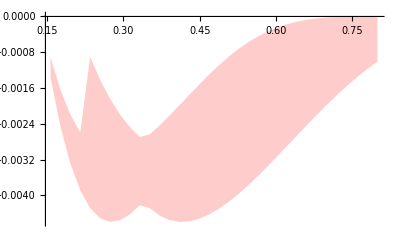

```mathematica
AULsinphi0errorbandY = ErrorBand[AULsinphi0funcY,0.02,0.8,40,Red]
```

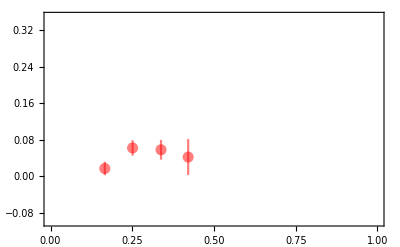

```mathematica
Clear[data,tab];
datapi0=Cases[Import["./data/pi0-eg1dvcs/pi0-aul-sin-x-dep4.dat","Table"],{_?NumberQ,___}]; 
tabpi0 =  Table[{{datapi0[[i]][[3]],datapi0[[i]][[4]]},ErrorBar[Sqrt[datapi0[[i]][[5]]^2+datapi0[[i]][[6]]^2]]},{i,1,4(*Length[datapip]*)}];
plotdataAULpi0=ErrorListPlot[tabpi0, Frame-> True,PlotRange->{{0,1},{-0.1,0.35}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

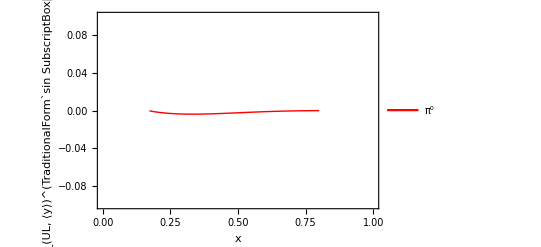

```mathematica
AULsinphilotY = Plot[{(AULsinphiY["pi+",x,0.5,2.,0.4]+AULsinphiY["pi-",x,0.5,2.,0.4])/2},{x,0.01,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.1,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_(UL, ⟨y⟩)^(TraditionalForm`sin SubscriptBox[Φ, h])"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^0"},{0.7,0.7}]]
```

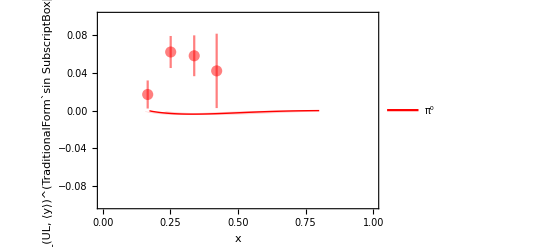

```mathematica
Show[AULsinphilotY,plotdataAULpi0,AULsinphi0errorbandY]
```

```mathematica
Export["../tex/figs/AULsinphi_JLAB_x.pdf",%,Background->None]
```

../tex/figs/AULsinphi_JLAB_x.pdf

Phenomenology of sub-leading twist spin asymmetry A_LL^cos[Φ_h]

## F_LL^cos[Φ_h] analytical result:

```mathematica
Print["Eq(3.3 e 4.2 c)(2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1], x g_L^⊥ = g1" ]
PTweightLLcosphih[PhT_] :=1;
```

Eq(3.3 e 4.2 c)(2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1], x g_L^⊥ = g1

```mathematica
Print["Eq(3.3 e 4.2 c)   F_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1] ="  ]
-(2 M)/Q ConvolutionTMD[omega1B, g1,D1]
```

Eq(3.3 e 4.2 c)   F_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1^2 z^2)) g_1 k_Tg1^2 P_hT z)/(π Q (p_TA^2+k_Tg1^2 z^2)^2)

```mathematica
Print["Eq(3.3 e 4.2 c)  ∫ⅆ^2P_hT F_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1] ="  ]
-(2 M)/Q PTConvolutionTMD[PTweightLLcosphih,omega1B,  g1,D1]
```

Eq(3.3 e 4.2 c)  ∫ⅆ^2P_hT F_LL^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/M(-x g_L^⊥)D_1] =

-(D_1 g_1 k_Tg1^2 √π z √(1/(p_TA^2+k_Tg1^2 z^2)))/Q

## F_LL^cos[Φ_h] numerics:

```mathematica
(*Eq. 7.5a*)

avLLcosphiPT[z_]:= avp+avkg z^2;

GfactorLLcosphi[z_,PT_] := avkg/(π avLLcosphiPT[z]^2) Exp[(-PT^2/avLLcosphiPT[z])]
AfactorLLcosphi[z_] := (z √Pi avkg)/(2 Mp √avLLcosphiPT[z]) ; 

FLLcosphi[pion_,x_,z_,Q2_,PT_] := (-(2 Mp)/Sqrt[Q2])(z PT)/Mp((4.0/9.0)g1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1sbar[x,Q2] D1sbar[pion,z,Q2] )GfactorLLcosphi[z,PT]

(*Eq. 7.5b*)

FLLcosphiIntegrated[pion_,x_,z_,Q2_] := (-(2 Mp)/Sqrt[Q2])((4.0/9.0)g1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1sbar[x,Q2] D1sbar[pion,z,Q2] )AfactorLLcosphi[z]
```

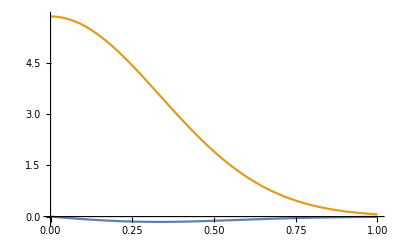

```mathematica
Plot[{FLLcosphi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_LL^cos[Φ_h]numerics:

```mathematica
ALLcosphi[pion_,x_,z_,Q2_,PT_] := FLLcosphi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

ALLcosphiIntegrated[pion_,x_,z_,Q2_] := FLLcosphiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS NEW

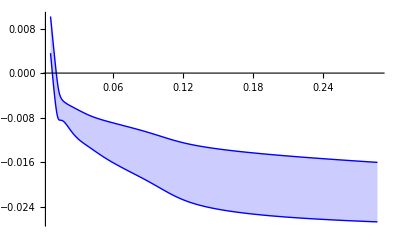

```mathematica
ALLcosphipimerrorband =ErrorBandCOMPASS[ALLcosphi,"pi-",Blue,"./bakur/ALLcosphi_compass_x_pim.csv"]
centralpim = central;
```

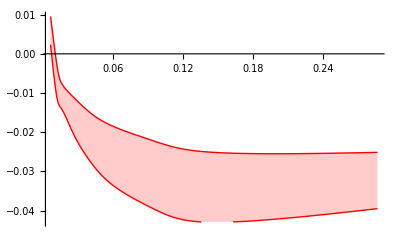

```mathematica
ALLcosphipiperrorband =ErrorBandCOMPASS[ALLcosphi,"pi+",Red,"./bakur/ALLcosphi_compass_x_pip.csv"]
centralpip = central;
```

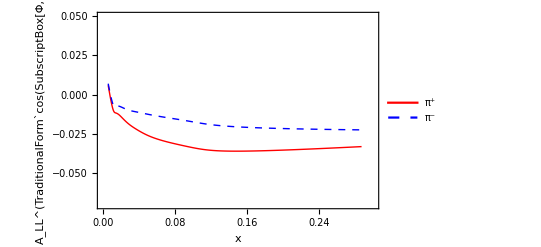

```mathematica
ALLcosphipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_LL^(TraditionalForm`cos(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.85,0.75}]]
```

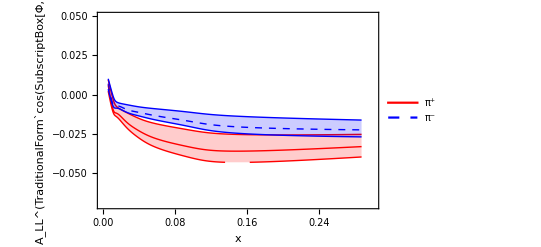

```mathematica
Show[ALLcosphipiplot,ALLcosphipiperrorband,ALLcosphipimerrorband]
```

```mathematica
Export["../tex/figs/ALLcosphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALLcosphi_COMPASS_x.pdf

Phenomenology of sub-leading twist spin asymmetry A_LT^cos[2 Φ_h-Φ_S]

## F_LT^cos[2 Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(4.2 d)(2 M)/QC[ -(2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1], x g_T^⊥ = g_(1  T)^⊥" ]
omega2C[kt_,PhT_,phi_] := (2(kt Cos[phi])^2-kt^2)/(2 M^2);
PTweightLTcos2phih[PhT_] :=1;
```

Eq(4.2 d)(2 M)/QC[ -(2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1], x g_T^⊥ = g_(1  T)^⊥

```mathematica
Print["Eq(4.2 d)   F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] ="  ]
-(2 M)/Q ConvolutionTMD[omega2C, gTperp,D1]
```

Eq(4.2 d)   F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+ktgT z^2)) gTperpSecondMoment M^3 P_hT^2 z^2)/(π Q (p_TA^2+ktgT z^2)^3)

```mathematica
XMomentTMD[2,gTperp]
```

ConditionalExpression[gTperpSecondMoment,Re[ktgT]>0]

```mathematica
XMomentTMD[0,g1T]
```

ConditionalExpression[(2 g_T^FIRST M^2)/k_Tg1T^2,Re[k_Tg1T^2]>0]

```mathematica
XMomentTMD[0,gTperp]
```

ConditionalExpression[(2 gTperpSecondMoment M^4)/ktgT^2,Re[ktgT]>0]

So that relation of gTperp (2) and g1Tperp is gTperpSecondMoment = (k_Tg1T^2 g_T^FIRST)/M^2

```mathematica
Print["Eq(4.2 d)  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] ="  ]
-(2 M)/Q PTConvolutionTMD[PTweightLTcos2phih,omega2C,  gTperp,D1]
```

Eq(4.2 d)  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] =

ConditionalExpression[-(2 D_1 gTperpSecondMoment M^3 z^2)/(Q (p_TA^2+ktgT z^2)),Re[p_TA^2+ktgT z^2]>0]

## F_LT^cos[2 Φ_h-Φ_S] analytical result(directly from WW):

```mathematica
Print["Eq(4.2 d)(2 M)/QC[ -(2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1], x g_T^⊥ = g_(1  T)^⊥" ]
PTweightLTcos2phih[PhT_] :=1;
```

Eq(4.2 d)(2 M)/QC[ -(2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1], x g_T^⊥ = g_(1  T)^⊥

```mathematica
Print["Eq(4.2 d)   F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] ="  ]
-(2 M)/Q ConvolutionTMD[omega2C, g1T,D1]
```

Eq(4.2 d)   F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] =

-(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+k_Tg1T^2 z^2)) g_T^FIRST k_Tg1T^2 M P_hT^2 z^2)/(π Q (p_TA^2+k_Tg1T^2 z^2)^3)

So that relation of gTperp (2) and g1Tperp is gTperpSecondMoment = (k_Tg1T^2 g_T^FIRST)/M^2 and the result is the same as above

```mathematica
Print["Eq(4.2 d)  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] ="  ]
(2 M)/Q PTConvolutionTMD[PTweightLTcos2phih,omega2C,  g1T,D1]
```

Eq(4.2 d)  ∫ⅆ^2P_hT F_LT^(TraditionalForm`cos[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])x g_T^⊥D_1] =

ConditionalExpression[(2 D_1 g_T^FIRST k_Tg1T^2 M z^2)/(Q (p_TA^2+k_Tg1T^2 z^2)),Re[p_TA^2+k_Tg1T^2 z^2]>0]

## F_LT^cos[2 Φ_h-Φ_S] numerics:

```mathematica
avkg1T = avkg; (*assumption*)
avLTcos2phiPT[z_]:= avp+avkg1T z^2;

GLTcos2phi[z_,PT_] := (Mp^2 avkg1T)/(π avLTcos2phiPT[z]^3) Exp[(-PT^2/avLTcos2phiPT[z])]
AfactorLTcos2phi[z_] := -(z^2 avkg1T)/avLTcos2phiPT[z]  

FLTcos2phi[pion_,x_,z_,Q2_,PT_] := ((2 Mp)/Sqrt[Q2])(-(z^2 PT^2)/Mp^2)((4.0/9.0)g1Tperpu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1Tperpd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1Tperps[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1Tperpubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1Tperpdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1Tperpsbar[x,Q2] D1sbar[pion,z,Q2] ) GLTcos2phi[z,PT]


FLTcos2phiIntegrated[pion_,x_,z_,Q2_] := ((2 Mp)/Sqrt[Q2])((4.0/9.0)g1Tperpu[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)g1Tperpd[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)g1Tperps[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)g1Tperpubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)g1Tperpdbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)g1Tperpsbar[x,Q2] D1sbar[pion,z,Q2] ) AfactorLTcos2phi[z]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.11061486030073391061134824298051171354018151760101318359375}. NIntegrate obtained -0.0262016 and 3.01517×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.120682927156044721150873755277643795125186443328857421875}. NIntegrate obtained -0.169845 and 1.84949×10^-7 for the integral and error estimates.

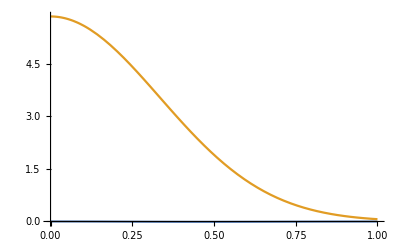

```mathematica
Plot[{FLTcos2phi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_LT^cos[2 Φ_h-Φ_S]numerics:

```mathematica
ALTcos2PhiminusPhiS[pion_,x_,z_,Q2_,PT_] := FLTcos2phi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

ALTcos2PhiminusPhiSIntegrated[pion_,x_,z_,Q2_] := FLTcos2phiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS NEW

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

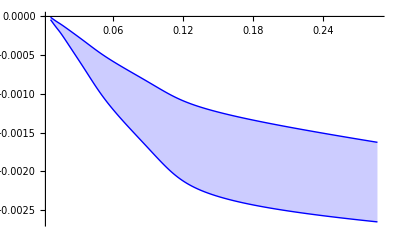

```mathematica
ALTcos2PhiminusPhiSpimerrorband =ErrorBandCOMPASS[ALTcos2PhiminusPhiS,"pi-",Blue,"./bakur/ALTcos2PhiminusPhiS_compass_x_pim.csv"]
centralpim = central;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained 8.26376 and 0.0023887 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.03588 and 0.00527687 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0128486}. NIntegrate obtained -7.0285 and 0.00941914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

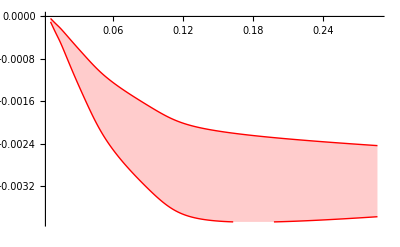

```mathematica
ALTcos2PhiminusPhiSpiperrorband =ErrorBandCOMPASS[ALTcos2PhiminusPhiS,"pi+",Red,"./bakur/ALTcos2PhiminusPhiS_compass_x_pip.csv"]
centralpip = central;
```

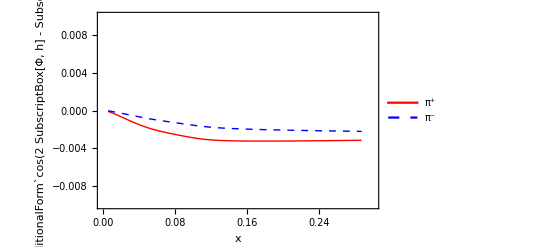

```mathematica
ALTcos2PhiminusPhiSpiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.01,0.01}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_LT^(TraditionalForm`cos(2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.85,0.75}]]
```

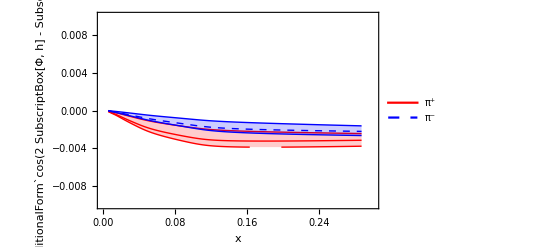

```mathematica
Show[ALTcos2PhiminusPhiSpiplot,ALTcos2PhiminusPhiSpiperrorband,ALTcos2PhiminusPhiSpimerrorband]
```

```mathematica
Export["../tex/figs/ALTcos2PhiminusPhiS_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/ALTcos2PhiminusPhiS_COMPASS_x.pdf

Phenomenology of subleading twist spin asymmetry A_UU^cos[Φ_h]

## F_UU^cos[Φ_h] analytical result:

```mathematica
Print["Eq(4.2 f)(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥-(h̄)/Mxf^⊥ D_1], xh = -2SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2]) h_1^⊥, xf^⊥ = f_1" ]

PTweightUUcosphih[PhT_] :=1;
```

Eq(4.2 f)(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥-(h̄)/Mxf^⊥ D_1], xh = -2SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2]) h_1^⊥, xf^⊥ = f_1

```mathematica
Print["Eq(4.2 f)   F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥] ="  ]
(2 M)/Q xBj ConvolutionTMD[omega1A, h,H1perp]
```

Eq(4.2 f)   F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+kth z^2)) h H_1^(FIRST perp) M M_hadron P_hT xBj z)/(π Q (p_TCOLLINS^2+kth z^2)^2)

```mathematica
Print["Eq(4.2 f)  ∫ⅆ^2P_hT F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥] ="  ]
(2 M)/Q xBj PTConvolutionTMD[PTweightUUcosphih,omega1A, h,H1perp]
```

Eq(4.2 f)  ∫ⅆ^2P_hT F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[ (h̄)/(z SubscriptBox[M, h])xh H_1^⊥] =

ConditionalExpression[(2 h H_1^(FIRST perp) M M_hadron √π xBj z)/(Q √(p_TCOLLINS^2+kth z^2)),p_TCOLLINS^2+z^2 Re[kth]>0]

```mathematica
Print["Eq(4.2 f)   F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ -(h̄)/Mxf^⊥ D_1] ="  ]
-(2 M)/Q xBj ConvolutionTMD[omega1B, fperp,D1]
```

Eq(4.2 f)   F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= (2 M)/QC[ -(h̄)/Mxf^⊥ D_1] =

-(4 D_1 ⅇ^(-P_hT^2/(p_TA^2+ktf z^2)) fperpFirstMoment M^2 P_hT xBj z)/(π Q (p_TA^2+ktf z^2)^2)

```mathematica
Print["Eq()  ∫ⅆ^2P_hT F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[  -(h̄)/Mxf^⊥ D_1] ="  ]
-(2 M)/Q PTConvolutionTMD[PTweightUUcosphih,omega1B, fperp,D1]
```

Eq()  ∫ⅆ^2P_hT F_UU^(TraditionalForm`cos[SubscriptBox[Φ, h]])= ∫ⅆ^2P_hT(2 M)/QC[  -(h̄)/Mxf^⊥ D_1] =

ConditionalExpression[-(2 D_1 fperpFirstMoment M^2 √π z √(1/(p_TA^2+ktf z^2)))/Q,Re[p_TA^2+ktf z^2]>0]

## F_UU^cos[Φ_h] numerics:

```mathematica
(*Eq. 7.9a*)

avUUcosphi2PT[z_]:= avp+avk z^2;
GfactorUUcosphi2[z_,PT_] := 1/(π avUUcosphi2PT[z]) Exp[(-PT^2/avUUcosphi2PT[z])]
AfactorUUcosphi2[z_] := (z √Pi avk)/(2 Mp  √avUUcosphi2PT[z]) ;

FUUcosphi[pion_,x_,z_,Q2_,PT_] := (-(2 Mp)/Sqrt[Q2])(z PT 2 Mp)/avUUcosphi2PT[z] avk/(2 Mp^2)((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sdbar[x,Q2]D1sbar[pion,z,Q2])GfactorUUcosphi2[z,PT]

(*Eq. 7.9b*)
FUUcosphiIntegrated[pion_,x_,z_,Q2_] := 
(-(2 Mp)/Sqrt[Q2])((4.0/9.0)f1u[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1d[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1s[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1ubar[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1dbar[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1sdbar[x,Q2]D1sbar[pion,z,Q2])AfactorUUcosphi2[z]
```

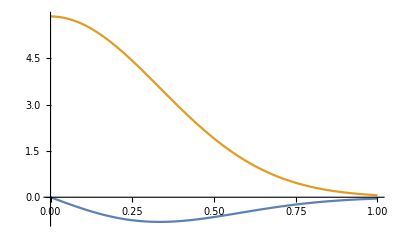

```mathematica
Plot[{FUUcosphi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UU^cos[Φ_h]numerics:

```mathematica
AUUcosphi[pion_,x_,z_,Q2_,PT_] := FUUcosphi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUUcosphiIntegrated[pion_,x_,z_,Q2_] := FUUcosphiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of PT dependence COMPASS

```mathematica
xcom = 0.05; zcom = 0.36; Q2com = (2. 160 Mp) xcom 0.35;
```

```mathematica
AUUcosphiPTpimfunc[PT_] :=AUUcosphi["pi-",xcom,zcom,Q2com,PT];
AUUcosphiPTpipfunc[PT_] :=AUUcosphi["pi+",xcom,zcom,Q2com,PT];
```

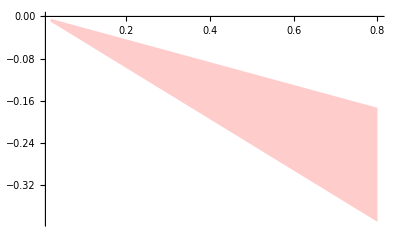

```mathematica
AUUcosphiPTpiperrorband = ErrorBand[AUUcosphiPTpipfunc,0.02,0.8,40,Red]
```

```mathematica
ErrorBandPrint[AUUcosphiPTpipfunc,0.02,0.8,40,"./bakur/AUUcosphi_compass_PT_pip.csv"]
```

{./bakur/AUUcosphi_compass_PT_pip.csv}

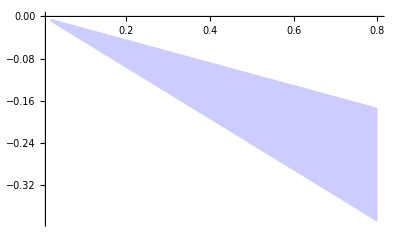

```mathematica
AUUcosphiPTpimerrorband = ErrorBand[AUUcosphiPTpimfunc,0.02,0.8,40,Blue]
```

```mathematica
ErrorBandPrint[AUUcosphiPTpimfunc,0.02,0.8,40,"./bakur/AUUcosphi_compass_PT_pim.csv"]
```

{./bakur/AUUcosphi_compass_PT_pim.csv}

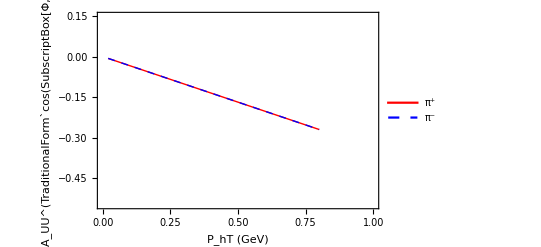

```mathematica
AUUcosphiPTpiplot = Plot[{AUUcosphiPTpipfunc[x],AUUcosphiPTpimfunc[x]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.55,0.15}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UU^(TraditionalForm`cos(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.7,0.75}]]
```

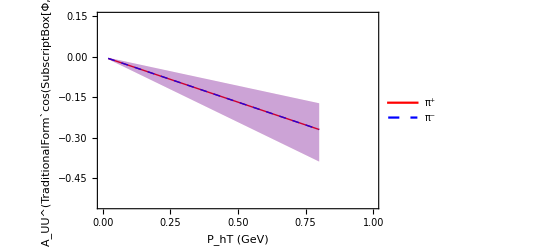

```mathematica
Show[AUUcosphiPTpiplot,AUUcosphiPTpiperrorband,AUUcosphiPTpimerrorband]
```

```mathematica
Export["../tex/figs/AUUcosphi_COMPASS_PT.pdf",%,Background->None]
```

../tex/figs/AUUcosphi_COMPASS_PT.pdf

### Plot of x dependence COMPASS NEW

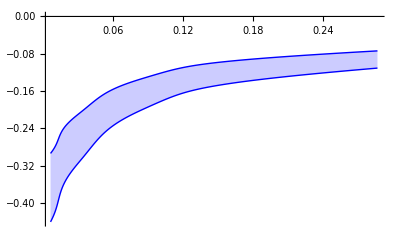

```mathematica
AUUcosphipimerrorband =ErrorBandCOMPASS[AUUcosphi,"pi-",Blue,"./bakur/AUUcosphi_compass_x_pim.csv"]
centralpim = central;
```

```mathematica
centralpim
```

{{0.006,-0.366825},{0.011,-0.341797},{0.016,-0.30613},{0.026,-0.27158},{0.04,-0.236009},{0.063,-0.190447},{0.101,-0.151445},{0.163,-0.118873},{0.287,-0.0921992}}

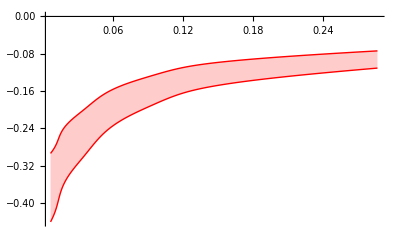

```mathematica
AUUcosphipiperrorband =ErrorBandCOMPASS[AUUcosphi,"pi+",Red,"./bakur/AUUcosphi_compass_x_pip.csv"]
centralpip = central;
```

```mathematica
centralpip
```

{{0.006,-0.366825},{0.011,-0.341797},{0.016,-0.30613},{0.026,-0.27158},{0.04,-0.236009},{0.063,-0.190447},{0.101,-0.151445},{0.163,-0.118873},{0.287,-0.0921992}}

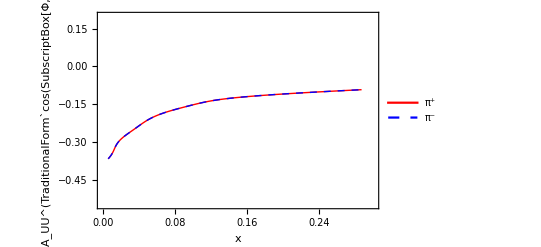

```mathematica
AUUcosphipiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.55,0.2}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UU^(TraditionalForm`cos(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.85,0.85}]]
```

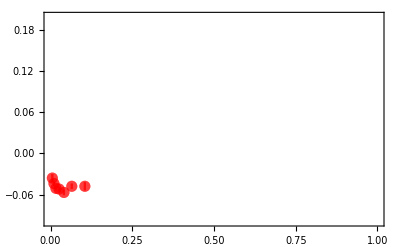

```mathematica
Clear[datapip,tabpip];
datapip=Cases[Import["./data/data-COMPASS-AUUcosphi","Table"],{_?NumberQ,___}]; 
tabpip =  Table[{{(datapip[[i]][[1]]+datapip[[i]][[2]])/2,datapip[[i]][[3]]},ErrorBar[datapip[[i]][[4]]]},{i,Length[datapip]},{j,1}];
plotdataAUUpip=ErrorListPlot[tabpip, Frame-> True,PlotRange->{{0,1},{-0.1,0.2}}, PlotStyle->{{Red,PointSize[0.02],Opacity[0.5]}}]
```

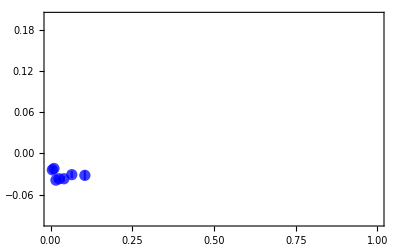

```mathematica
Clear[datapim,tabpim];
datapim=Cases[Import["./data/data-COMPASS-AUUcosphi","Table"],{_?NumberQ,___}]; 
tabpim =  Table[{{(datapim[[i]][[1]]+datapim[[i]][[2]])/2,datapim[[i]][[5]]},ErrorBar[datapim[[i]][[6]]]},{i,Length[datapim]},{j,1}];
plotdataAUUpim=ErrorListPlot[tabpim, Frame-> True,PlotRange->{{0,1},{-0.1,0.2}}, PlotStyle->{{Blue,PointSize[0.02],Opacity[0.5]}}]
```

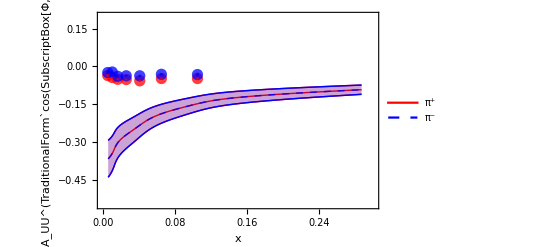

```mathematica
Show[AUUcosphipiplot,AUUcosphipiperrorband,AUUcosphipimerrorband, plotdataAUUpip,plotdataAUUpim]
```

```mathematica
Export["../tex/figs/AUUcosphi_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUUcosphi_COMPASS_x.pdf

Phenomenology of subleading twist spin asymmetry A_UT^sin[Φ_S]

## F_UT^sin[Φ_S] analytical result:

```mathematica
Print["Eq(4.2 g)(2 M)/QC[ xf_T D_1-p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥], xf_T = -SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2]) f_(1  T)^⊥, xh_T-xh_T^⊥ = -2 h_1 " ]
(* weightUTsinphih1[kt_,PhT_,phi_] := 1;
weightUTsinphih2[kt_,PhT_,phi_] := -1/(2 z M Mhadron)(kt PhT Cos[phi] - z kt kt); *)

PTweightUTsinphih[PhT_] :=1;
```

Eq(4.2 g)(2 M)/QC[ xf_T D_1-p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥], xf_T = -SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2]) f_(1  T)^⊥, xh_T-xh_T^⊥ = -2 h_1

```mathematica
Print["Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ xf_T D_1] ="  ]
(2 M)/Q ConvolutionTMD[omega0, fT,D1]
```

Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ xf_T D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+ktfT z^2)) fT M)/(Q (π p_TA^2+ktfT π z^2))

```mathematica
Print["Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ xf_T D_1] ="  ]
(2 M)/Q PTConvolutionTMD[PTweightUTsinphih,omega0, fT,D1]
```

Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[ xf_T D_1] =

ConditionalExpression[(2 D_1 fT M)/Q,Re[p_TA^2+ktfT z^2]>0]

```mathematica
Print["Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] ="  ]
(2 M)/Q(-xBj/2)ConvolutionTMD[omega2B, hT,H1perp]
```

Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] =

-(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1^2 z^2)) H_1^(FIRST perp) hTFirstMoment M^2 M_hadron xBj z^2 (-P_hT^2+p_TCOLLINS^2+k_Th1^2 z^2))/(π Q (p_TCOLLINS^2+k_Th1^2 z^2)^3)

```mathematica
Print["Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] ="  ]
-(2 M)/Q(-xBj/2)ConvolutionTMD[omega2B, hTperp,H1perp]
```

Eq(4.2 g)   F_UT^(TraditionalForm`sin[SubscriptBox[Φ, S]])= (2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1^2 z^2)) H_1^(FIRST perp) hTperpFirstMoment M^2 M_hadron xBj z^2 (-P_hT^2+p_TCOLLINS^2+k_Th1^2 z^2))/(π Q (p_TCOLLINS^2+k_Th1^2 z^2)^3)

```mathematica
Print["Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, hS]])= ∫ⅆ^2P_hT(2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] ="  ]
(2 M)/Q(-xBj/2)PTConvolutionTMD[PTweightUTsinphih,omega2B, hT,H1perp]
```

Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, hS]])= ∫ⅆ^2P_hT(2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] =

0

```mathematica
Print["Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, hS]])= ∫ⅆ^2P_hT(2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] ="  ]
-(2 M)/Q(-xBj/2)PTConvolutionTMD[PTweightUTsinphih,omega2B, hTperp,H1perp]
```

Eq(4.2 g)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[SubscriptBox[Φ, hS]])= ∫ⅆ^2P_hT(2 M)/QC[ -p_T/(2 z SubscriptBox[M, h] M)(xh_T-xh_T^⊥) H_1^⊥] =

0

## F_UT^sin[Φ_S] numerics:

```mathematica
avkh1 = avk; (*asumption*)
avc = MC^2 avp/(MC^2 + avp);
avUTsinphi2PT[z_]:= avc+avkh1 z^2;
GfactorUTsinphi2[z_,PT_] := (1-PT^2/avUTsinphi2PT[z])/(π avUTsinphi2PT[z]) Exp[(-PT^2/avUTsinphi2PT[z])]
AfactorUTsinphi2[z_] := 0. ;

FUTsinphiS[pion_,x_,z_,Q2_,PT_] := ((2 Mp)/Sqrt[Q2])(4 z^2 Mh Mp)/avUTsinphi2PT[z] avkh1/(2 Mp^2)((4.0/9.0)h1u[x,Q2] If[pion=="pi+",H1perpFavFirstMoment[z,Q2],H1perpUnfFirstMoment[z,Q2]] +(1.0/9.0)h1d[x,Q2] If[pion=="pi+",H1perpUnfFirstMoment[z,Q2],H1perpFavFirstMoment[z,Q2]])GfactorUTsinphi2[z,PT]


FUTsinphiSIntegrated[pion_,x_,z_,Q2_] := 0
```

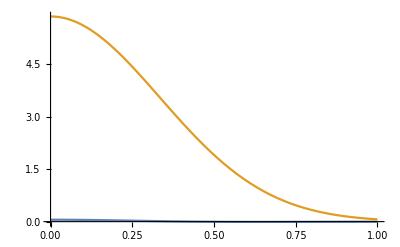

```mathematica
Plot[{FUTsinphiS["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UT^sin[Φ_S]numerics:

```mathematica
AUTsinphiS[pion_,x_,z_,Q2_,PT_] := FUTsinphiS[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUTsinphiSIntegrated[pion_,x_,z_,Q2_] := FUTsinphiSIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS NEW

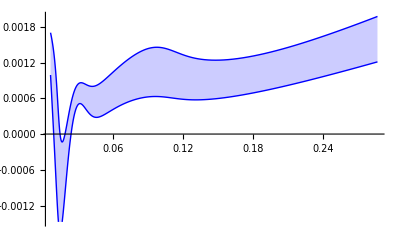

```mathematica
AUTsinphiSpimerrorband =ErrorBandCOMPASS[AUTsinphiS,"pi-",Blue,"./bakur/AUTsinphiS_compass_x_pim.csv"]
centralpim = central;
```

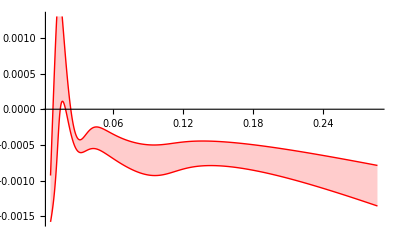

```mathematica
AUTsinphiSpiperrorband =ErrorBandCOMPASS[AUTsinphiS,"pi+",Red,"./bakur/AUTsinphiS_compass_x_pip.csv"]
centralpip = central;
```

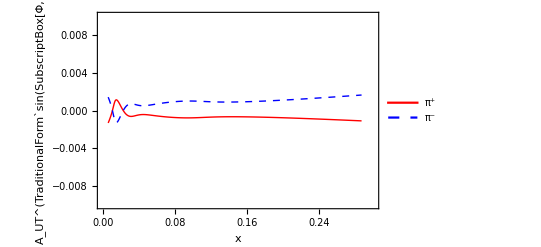

```mathematica
AUTsinphiSpiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.01,0.01}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.85,0.85}]]
```

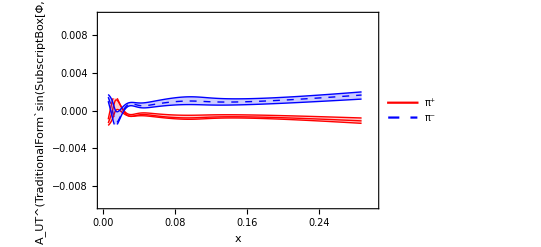

```mathematica
Show[AUTsinphiSpiplot,AUTsinphiSpiperrorband,AUTsinphiSpimerrorband]
```

```mathematica
Export["../tex/figs/AUTsinphiS_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUTsinphiS_COMPASS_x.pdf

Phenomenology of subleading twist spin asymmetry A_UT^sin[2 Φ_h-Φ_S]

## F_UT^sin[2 Φ_h-Φ_S] analytical result:

```mathematica
Print["Eq(4.2 h)(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1+(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥], xf_T^⊥ =  f_(1  T)^⊥, xh_T+xh_T^⊥ = -2 SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2])h_(1  T)^⊥ " ]
PTweightUTsin2phih[PhT_] :=1;
```

Eq(4.2 h)(2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1+(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥], xf_T^⊥ =  f_(1  T)^⊥, xh_T+xh_T^⊥ = -2 SubsuperscriptBox[k, T, 2]/(2 SuperscriptBox[M, 2])h_(1  T)^⊥

```mathematica
Print["Eq(4.2 h)   F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1] ="  ]
(2 M)/Q xBj ConvolutionTMD[omega2C, fTperp,D1]
```

Eq(4.2 h)   F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1] =

(2 D_1 ⅇ^(-P_hT^2/(p_TA^2+ktfT z^2)) fTperpSecondMoment M^3 P_hT^2 xBj z^2)/(π Q (p_TA^2+ktfT z^2)^3)

```mathematica
Print["Eq(4.2 h)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1] ="  ]
(2 M)/Q xBj PTConvolutionTMD[PTweightUTsin2phih,omega2C, fTperp,D1]
```

Eq(4.2 h)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[ (2 SuperscriptBox[(OverscriptBox[h, _] . SubscriptBox[k, T]), 2] - SuperscriptBox[SubscriptBox[k, T], 2])/(2 SuperscriptBox[M, 2])xf_T^⊥ D_1] =

ConditionalExpression[(2 D_1 fTperpSecondMoment M^3 xBj z^2)/(Q (p_TA^2+ktfT z^2)),Re[p_TA^2+ktfT z^2]>0]

```mathematica
Print["Eq(4.2 h)   F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥] ="  ]
(2 M)/Q xBj 1/2 ConvolutionTMD[omega2AB, hT,H1perp]
```

Eq(4.2 h)   F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= (2 M)/QC[(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥] =

(4 ⅇ^(-P_hT^2/(p_TCOLLINS^2+k_Th1^2 z^2)) H_1^(FIRST perp) hTFirstMoment M^2 M_hadron P_hT^2 xBj z^2)/(π Q (p_TCOLLINS^2+k_Th1^2 z^2)^3)

```mathematica
Print["Eq(4.2 h)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥] ="  ]
(2 M)/Q xBj 1/2 PTConvolutionTMD[PTweightUTsin2phih,omega2AB,  hT,H1perp]
```

Eq(4.2 h)  ∫ⅆ^2P_hT F_UT^(TraditionalForm`sin[2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]])= ∫ⅆ^2P_hT(2 M)/QC[(2 (OverscriptBox[h, _] . SubscriptBox[k, T]) (OverscriptBox[h, _] . SubscriptBox[p, T]) - SubscriptBox[p, T] . SubscriptBox[k, T])/(2 z M SubscriptBox[M, h])(xh_T+xh_T^⊥) H_1^⊥] =

(4 H_1^(FIRST perp) hTFirstMoment M^2 M_hadron xBj z^2)/(Q (p_TCOLLINS^2+k_Th1^2 z^2))

## F_UT^sin[2 Φ_h-Φ_S] numerics:

```mathematica
(*Eq. 7.8a*)

avUTsin2phi1PT[z_]:= avp+avks z^2;

GfactorUTsin2phi1[z_,PT_] := Mp^2/(π avUTsin2phi1PT[z]) Exp[(-PT^2/avUTsin2phi1PT[z])]
AfactorUTsin2phi1[z_] :=(Mp^2 z^2)/avUTsin2phi1PT[z] ; 

avkP = avk MTT^2/(avk+MTT^2);
avc = MC^2 avp/(MC^2 + avp);
avUTsin2phi2PT[z_]:= avc+avkP z^2;
GfactorUTsin2phi2[z_,PT_] :=1/(π avUTsin2phi2PT[z]) Exp[(-PT^2/avUTsin2phi2PT[z])]
AfactorUTsin2phi2[z_] := (4 Mh Mp z^2)/avUTsin2phi1PT[z] ;

FUTsin2phi[pion_,x_,z_,Q2_,PT_] := ((2 Mp)/Sqrt[Q2])(z^2 PT^2)/avUTsin2phi1PT[z]^2 avks/Mp^2((4.0/9.0)f1TperpuFirstMoment[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1TperpdFirstMoment[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1TperpsFirstMoment[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1TperpubarFirstMoment[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1TperpdbarFirstMoment[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1TperpsbFirstMoment[x,Q2] D1sbar[pion,z,Q2] )GfactorUTsin2phi1[z,PT] + ((2 Mp)/Sqrt[Q2])(z^2 PT^2 4Mp Mh)/avUTsin2phi2PT[z]^2(-1)((4.0/9.0)h1TperpuSecondMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1TperpdSecondMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2])GfactorUTsin2phi2[z,PT]

(*Eq. 7.8b*)
FUTsin2phiIntegrated[pion_,x_,z_,Q2_] := ((2 Mp)/Sqrt[Q2])avks/Mp^2((4.0/9.0)f1TperpuFirstMoment[x,Q2] D1u[pion,z,Q2] +(1.0/9.0)f1TperpdFirstMoment[x,Q2] D1d[pion,z,Q2]+(1.0/9.0)f1TperpsFirstMoment[x,Q2] D1s[pion,z,Q2]  + (4.0/9.0)f1TperpubarFirstMoment[x,Q2] D1ubar[pion,z,Q2]+(1.0/9.0)f1TperpdbarFirstMoment[x,Q2] D1dbar[pion,z,Q2] +(1.0/9.0)f1TperpsbFirstMoment[x,Q2] D1sbar[pion,z,Q2] )AfactorUTsin2phi1[z]+
((2 Mp)/Sqrt[Q2]) (-1)((4.0/9.0)h1TperpuSecondMoment[x,Q2] H1perpFirstMoment["u",pion,z,Q2] +(1.0/9.0)h1TperpdSecondMoment[x,Q2] H1perpFirstMoment["d",pion,z,Q2])AfactorUTsin2phi2[z]
```

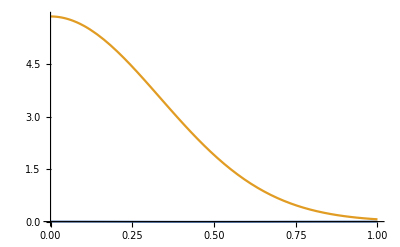

```mathematica
Plot[{FUTsin2phi["pi+",0.1,0.3,1,PT],FUU["pi+",0.1,0.3,1,PT]},{PT,0,1}]
```

## A_UT^sin[2 Φ_h-Φ_S]numerics:

```mathematica
AUTsin2PhiminusPhiS[pion_,x_,z_,Q2_,PT_] := FUTsin2phi[pion,x,z,Q2,PT]/FUU[pion,x,z,Q2,PT];

AUTsin2PhiminusPhiSIntegrated[pion_,x_,z_,Q2_] := FUTsin2phiIntegrated[pion,x,z,Q2]/FUUIntegrated[pion,x,z,Q2];
```

### Plot of x dependence COMPASS NEW

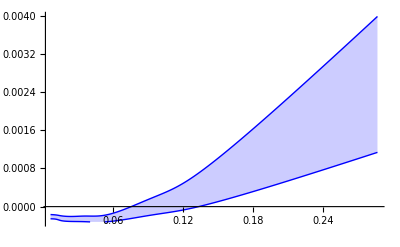

```mathematica
AUTsin2PhiminusPhiSpimerrorband =ErrorBandCOMPASS[AUTsin2PhiminusPhiS,"pi-",Blue,"./bakur/AUTsin2PhiminusPhiS_compass_x_pim.csv"]
centralpim = central;
```

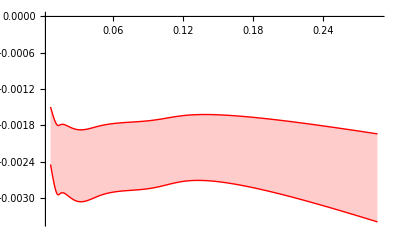

```mathematica
AUTsin2PhiminusPhiSpiperrorband =ErrorBandCOMPASS[AUTsin2PhiminusPhiS,"pi+",Red,"./bakur/AUTsin2PhiminusPhiS_compass_x_pip.csv"]
centralpip = central;
```

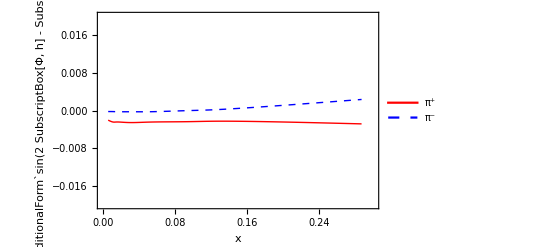

```mathematica
AUTsin2PhiminusPhiSpiplot = ListPlot[{centralpip,centralpim},Frame-> True,Joined-> True,InterpolationOrder->4,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,0.3},{-0.02,0.02}},PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Times New Roman"},LabelStyle->Directive[FontFamily->"Times New Roman"],PlotLegends->Placed[{"π^+","π^-"},{0.25,0.85}]]
```

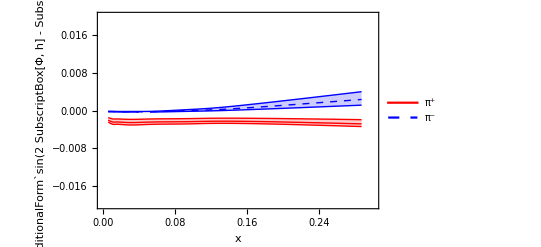

```mathematica
Show[AUTsin2PhiminusPhiSpiplot,AUTsin2PhiminusPhiSpiperrorband,AUTsin2PhiminusPhiSpimerrorband]
```

```mathematica
Export["../tex/figs/AUTsin2PhiminusPhiS_COMPASS_x.pdf",%,Background->None]
```

../tex/figs/AUTsin2PhiminusPhiS_COMPASS_x.pdf